# Modeling evolutionary rescue - Figure 1

## To reproduce Figure 1, first evaluate the subsection entitled “Simulation data,” then evaluate “Figure 1 code.”

### Simulation code

The simulation algorithm below is a variant of the algorithm outlined in the following manuscript:
Cao, Y., Gillespie, D.T., & Petzold, L.R. (2006). Efficient step size selection for the tau-leaping simulation method. The Journal of Chemical Physics, 124(4). https://doi.org/10.1063/1.2159468

```mathematica
TotalRuns=2; (*Number of replicate simulation runs*)
rho=2/100; (*Value by which the relative change in each event rate is bound*)
FiringsThreshold=10^3; (*Number of firings away from extinction at which a reaction is deemed "critical"*)
ReplicateNumber=0;

(*State change [1,j] on wild-type abundance due to each event j*)
StateChange[1,1]=1; (*Wild type gives birth*)
StateChange[1,2]=-1; (*Wild type dies*)
StateChange[1,3]=0; (*Mutant gives birth*)
StateChange[1,4]=0; (*Mutant dies*)
StateChange[1,5]=0; (*Mutation occurs*)

(*State change [2,j] on mutant abundance due to each event j*)
StateChange[2,1]=0; (*Wild type gives birth*)
StateChange[2,2]=0; (*Wild type dies*)
StateChange[2,3]=1; (*Mutant gives birth*)
StateChange[2,4]=-1; (*Mutant dies*)
StateChange[2,5]=1; (*Mutation occurs*)

(*Each ReactionList[i] holds the reactions that directly affect variable i, i.e., the reactions that cause variable i to decrease or increase in abundance.*)
ReactionList[1]={1,2};
ReactionList[2]={3,4,5};

(*We will want to know the order of the highest order reaction that each variable is involved in. Upon inspection, we see that this value is two for all variables.*)
HR[1]=HR[2]=2;

(*Total number of variables*)
NumberOfVariables=2;
```

```mathematica
(*Equilibrium*)
NAhat[b_,d_,deltab_,deltad_,K1_]:=K1;
```

```mathematica
(*Set the initial conditions for the tau-leaping simulations.*)
InitialConditions[K1_]:=Module[{},

(*We assume there are initially zero mutants present*)
V[1]=K1;
V[2]=0;

(*We initialize the process at t = 0.*)
t10=0;

(*Initial list of non-critical reactions, i.e, reactions whose affected variables have abundances > FiringsThreshold*)
NonCriticalReactions={1,2,3,4,5};

(*Make a static list of the indices corresponding to each reaction involved in the simulation.*)
AllReactions=Range[5];

(*Lists that store the i values of the three variables at each of the i time steps comprising a single simulation*)
TimeList={};
WildtypeList={};
MutantList={};
MutantFrequencyList={};
(*Integers we will use as increments for the lists holding the variables*)
J2=0;
J3=0;
J4=0;
J5=0;
J6=0;
]
```

```mathematica
(*A tau-leaping simulation that follows the algorithm described in Sections IIC and IV of Cao et al. (2006).*)
TauLeapingSimulation[sA_,sM_,K1_]:=Module[{},

(*Initialize*)
InitialConditions[K1];

(*Perform the simulation until either time tf is reached or the population goes extinct.*)
While[V[1]>1||0<V[2]<K1,

(*Update the list of non-critical reactions and reactant variables.*)
CriticalReactions={};
ReactantVariables={};
Do[

If[

V[i]<FiringsThreshold,

NonCriticalReactions=Complement[NonCriticalReactions,ReactionList[i]];

CriticalReactions=DeleteDuplicates[Join[CriticalReactions,ReactionList[i]]],

NonCriticalReactions=DeleteDuplicates[Join[NonCriticalReactions,ReactionList[i]]];

ReactantVariables=DeleteDuplicates[Join[ReactantVariables,{i}]]],

{i,1,NumberOfVariables}];

(*Propensity functions*)
Propensity[1]=V[1]*1; (*Wild type gives birth*)
Propensity[2]=V[1]*(1+sA); (*Wild type dies*)
Propensity[3]=V[2]*1; (*Mutant gives birth*)
Propensity[4]=V[2]*(1-sM); (*Mutant dies*)
Propensity[5]=V[1]*(1/10)/K1; (*Mutation occurs*)

(*If the number of non-critical variables is ≥ 1, calculate the first candidate time leap, Tau1, using Equation 33 in Cao et al. (2006). Otherwise, set Tau1 equal to infinity. If the first auxillary value for reaction j, Mu[j], is zero, add 0.000000001 to Mu[j] to avoid having zero in the denominator of the equation for Tau1.*)
If[

Length[ReactantVariables]≥1,

Do[

Mu[ReactantVariables[[i]]]=Sum[StateChange[ReactantVariables[[i]],NonCriticalReactions[[j]]]*Propensity[NonCriticalReactions[[j]]],

{j,1,Length[NonCriticalReactions]}];

If[

Mu[ReactantVariables[[i]]]==0,

Mu[ReactantVariables[[i]]]=Mu[ReactantVariables[[i]]]+0.000000001],

{i,1,Length[ReactantVariables]}];

Do[

SigmaSquared[ReactantVariables[[i]]]=Sum[StateChange[ReactantVariables[[i]],NonCriticalReactions[[j]]]^2*Propensity[NonCriticalReactions[[j]]],
{j,1,Length[NonCriticalReactions]}];

If[

SigmaSquared[ReactantVariables[[i]]]==0,

SigmaSquared[ReactantVariables[[i]]]=SigmaSquared[ReactantVariables[[i]]]+0.000000001],

{i,1,Length[ReactantVariables]}];

Tau1=Min[Table[Min[

{Max[rho*V[ReactantVariables[[i]]]/HR[ReactantVariables[[i]]],1]/Abs[Mu[ReactantVariables[[i]]]],

Max[rho*V[ReactantVariables[[i]]]/HR[ReactantVariables[[i]]],1]^2/SigmaSquared[ReactantVariables[[i]]]}],{i,1,Length[ReactantVariables]}]],

Tau1=Infinity];

(*Compute the sum of the critical propensity functions.*)
If[

Length[CriticalReactions]≥1,

SumOfCriticalPropensities=Sum[Propensity[CriticalReactions[[j]]],{j,1,Length[CriticalReactions]}];

(*Compute a second candidate time leap, Tau2, as a sample of the exponential random variable with mean 1/SumOfCriticalPropensities.*)
If[

SumOfCriticalPropensities>0,

Tau2=RandomVariate[ExponentialDistribution[SumOfCriticalPropensities]],

Tau2=Infinity],

Tau2=Infinity
];

(*Calculate the actual time leap, Tau. If Tau1 < Tau2, then Tau = Tau1. Otherwise, Tau = Tau2.*)
If[

Tau1<Tau2,

Tau = Tau1,

Tau=Tau2];

(*Let the number of firings for each non-critical reaction j be a sample of the Poisson random variable with mean Propensity[j]*Tau.*)
Do[

If[
Propensity[NonCriticalReactions[[j]]] ==0,

Firings[NonCriticalReactions[[j]]]=0,

Firings[NonCriticalReactions[[j]]]=RandomVariate[PoissonDistribution[Propensity[NonCriticalReactions[[j]]]*Tau]]],

{j,1,Length[NonCriticalReactions]}];

(*If Tau = Tau1, we set the number of firings for the critical reactions equal to zero.*)
If[

Tau==Tau1&&Length[CriticalReactions]≥1,

Do[

Firings[CriticalReactions[[j]]]=0,

{j,1,Length[CriticalReactions]}]];

(*If Tau = Tau2, a single critical reaction will fire once. Determine which critical reaction, X, will fire by taking a sample of the integer random variable with point probabilities Propensity[j]/SumOfCriticalPropensities, where j only runs over the index values of the critical reactions. The remaining critical reactions (i.e., those that are not reaction X) each fire zero times.*)
If[

Tau==Tau2&&Length[CriticalReactions]≥1,

ListOfProbabilities=Table[Propensity[CriticalReactions[[j]]]*Tau,

{j,1,Length[CriticalReactions]}];

Distribution1=EmpiricalDistribution[ListOfProbabilities->CriticalReactions];

X10=RandomVariate[Distribution1];

Firings[X10]=1;

CriticalReactionsExcludingX10=Complement[CriticalReactions,{X10}];

If[

Length[CriticalReactionsExcludingX10]≥1,

Do[

Firings[CriticalReactionsExcludingX10[[j]]]=0,

{j,1,Length[CriticalReactionsExcludingX10]}]]];

(*Calculate the updated values of V[1],V[2],and V[3].*)
Do[

Update1[i]=V[i]+Sum[Firings[AllReactions[[j]]]*StateChange[i,AllReactions[[j]]],{j,1,Length[AllReactions]}],

{i,1,NumberOfVariables}];

(*Determine whether any of the i updated values, Update[i], are negative. If a variable does have a negative abundance, set its abundance equal to zero.*)
Do[

If[

Update1[i]<0,

V[i]=0,

V[i]=Update1[i]],

{i,1,NumberOfVariables}];

(*Update time.*)
t10=t10+Tau;

(*Update variable lists.*)
J2=J2+1; 
J3=J3+1;
J4=J4+1;
J5=J5+1;

TimeList=Insert[TimeList,t10,J2];
WildtypeList=Insert[WildtypeList,V[1],J3];
MutantList=Insert[MutantList,V[2],J5];
MutantFrequencyList=Insert[MutantFrequencyList,V[2]/(V[1]+V[2]),J4];
];

(*Determine whether the final mutant abundance is > 0 (i.e., whether mutants survived). Print a 1 if mutants survived and a zero if not.*)
If[V[2]>0,V2Final=1,V2Final=0];

ReplicateNumber=ReplicateNumber+1;
Print["Simulation Number ",ReplicateNumber," ended with ", V[2], " mutants"]

]
```

### Simulation data

Data included:

List1[3,1]  = Time for failed mutant rescue
List1[1,1] = mutant abundance for failed rescue
List4[3,1] = Time for wild type abundance during failed rescue
List4[2,1] = wild type abundance during failed rescue

List5[3,1] = Time for failed mutant rescue (updated)
List5[2,1] = wild type abundance during failed rescue (updated)
List5[1,1] = mutant abundance during failed rescue (updated)

List2[3,1]  = Time for successful rescue
List2[1,1] = mutant abundance for successful rescue
List2[2,1] = wild type abundance for successful rescue

Mutant extinction case

```mathematica
List1[3,1]={0.000591224379346514,0.0010350593443879245,0.001136158548438844,0.001137448994444333,0.0015493955353383334,0.001705931324768333,0.001774821627325956,0.0026280633098389895,0.0032069429351559726,0.003344805498199602,0.0034583728186111753,0.0046746563344079155,0.0050654544475959625,0.005119490267792071,0.005234095957206872,0.006512881847369568,0.006523560072944807,0.006623803933240105,0.007054154611506,0.007101636130928131,0.008024074223213596,0.00979656924537743,0.009889416888482282,0.011803912581220917,0.012722417565561733,0.012812048159618918,0.014020628476271849,0.01749446911062576,0.017545172617917347,0.01768357742299588,0.019586081224275968,0.020459223093679993,0.020514910360143256,0.021628045088527396,0.021738427340879735,0.021931249738045666,0.02302226187808995,0.023034439669575968,0.026086205452065848,0.026255643424342348,0.027209908928820144,0.03165165633459761,0.03286333260135643,0.03441718669741766,0.03562709296268964,0.03659121895713468,0.036738625202151355,0.037361171785667203,0.037451229655132555,0.03778949018842368,0.03783647707057092,0.039083683462787205,0.039197772981889326,0.03923162055464469,0.0413018143243792,0.04243803941626672,0.04261167814750786,0.04311908935208198,0.04514132097759504,0.04581725856137769,0.04847063438990667,0.04861525940730872,0.049034302243135555,0.05124832909918637,0.05138784156336744,0.051798590009490844,0.052498184800419165,0.054923155575195844,0.05525889900215477,0.05533084605891493,0.055624297425700325,0.05613869569542305,0.05654472500095567,0.05811212359766947,0.059768791593696864,0.06192191746911307,0.061943086374205016,0.06279572259125728,0.06497273744886696,0.06578002370970096,0.06749035946866984,0.06954019977020387,0.07011890332444261,0.07087013504763648,0.07252006207455172,0.0746961731230004,0.07487296859420328,0.07511324701912261,0.07603848283735436,0.07606151475092424,0.07702756112741681,0.07727087522677036,0.07769363640876656,0.07819319490827224,0.07904295177753354,0.07937134681050857,0.07960565538100241,0.08077281850639495,0.08395987621318601,0.08581336812299507,0.08583660291042572,0.08598325275708014,0.08672160210029305,0.08757088041720609,0.08867539453926386,0.0892730737241467,0.08946597055626745,0.09011333653273361,0.09197122968347791,0.09255487140142891,0.09583955953187169,0.09771555894823666,0.09806786683703475,0.09996298454563238,0.10017225464545966,0.10042980536818849,0.10074736227490393,0.10295426294214512,0.10308512933755486,0.10335022204858524,0.10363817177438843,0.10537945340594074,0.10609196371903487,0.10915375329113844,0.10921894456792683,0.10945761982710733,0.11150918672583149,0.1128571359761298,0.1138077553464932,0.11428905591234406,0.1150530167216593,0.11617595181566916,0.11683034816424408,0.11932441380799291,0.11962556551719272,0.12027198961955722,0.12154715471255073,0.12187065414192663,0.12381271788909505,0.12556301941907203,0.12594206352721501,0.1264974942887534,0.12732481433216006,0.12774390202207572,0.12810047009604558,0.1288913960150987,0.1290071203617593,0.13033837809892138,0.13062090199087406,0.1321554763013248,0.13327516120994348,0.1356222924896613,0.13624602302602057,0.13694215800863424,0.13822129114358797,0.13964167561384028,0.14052832421230946,0.14167699262893746,0.1424228039842288,0.14252615883114805,0.1430976518957892,0.14336143355348352,0.14379711625136155,0.14561912132563082,0.1465306637158121,0.14668124841000493,0.14711038932742934,0.14781530478404187,0.1486151523858028,0.1500324255897282,0.15008422398218893,0.1522000941905977,0.1526956651003285,0.15355267431850297,0.15500308022879225,0.15529389380519187,0.15553802462777844,0.15621486405968263,0.16065096221584416,0.16247087568363627,0.16265810120463023,0.16288696180315293,0.16417187168640643,0.1651013584350204,0.16867160554751448,0.16953770838069643,0.16960001082040319,0.1711093621788627,0.17119182316530532,0.17129682202037624,0.1731991194023655,0.17368483839584564,0.1738191773617876,0.17408954438993984,0.17439847035714393,0.17551471316135758,0.17651500014014335,0.1769567643639102,0.17800215885231235,0.17950845112046768,0.17966801186800035,0.18020810083904162,0.18138021766788787,0.181434424347591,0.1814379667194113,0.18365990350986122,0.18464158656160326,0.18591555775091953,0.18651857661527818,0.1878510222348097,0.18915606550511124,0.1916250789703672,0.19201686587252717,0.19335252414576307,0.1934986026178236,0.19365466159792605,0.19386779458416173,0.19547023666055627,0.19610548980278927,0.19682431844199672,0.1969298351848202,0.19766898835553431,0.19778402939645537,0.19790471205175192,0.1981811948853287,0.1982248584513275,0.19824093927931893,0.19972222388135363,0.20039228479845572,0.20276829209879738,0.2037176777902889,0.20439734409045676,0.20486844543538762,0.20496801337396994,0.20584508168580948,0.20591320630568116,0.2059276741077844,0.20611512851102326,0.206338389544812,0.20654324730761683,0.20890896541561652,0.20893390080912452,0.20946592840106346,0.20955159273130475,0.21152844372391982,0.21479702369789022,0.21667457286999933,0.21808418848520902,0.2185029511443947,0.21873281664869043,0.21982645955380384,0.22346350989690691,0.22359372023322807,0.2240365405096244,0.2252678399583398,0.22533538084119134,0.22537407124922174,0.22666088725034747,0.23129099266556719,0.2322246774898263,0.23308665794404332,0.23362557554300564,0.23534335077358093,0.23576630026808504,0.2358658426678606,0.2363555207862596,0.23638355096082259,0.23652373588768746,0.237890372331456,0.24054482239895192,0.24068728509740545,0.24416070939585482,0.2450433275254535,0.2455911643441245,0.2471114114821695,0.24718260391933694,0.24727745367445939,0.24753241493326786,0.2486621044567526,0.24948195002627804,0.2522940360986758,0.2526489675218398,0.2533850013975246,0.2540765189969041,0.2566540613015341,0.2577534547519153,0.2579681634797243,0.25855337444246057,0.25895732864034093,0.2609047493200476,0.2625009888148124,0.26278420087455273,0.2628048178104556,0.26303387612404056,0.26317594989675985,0.2632156051873282,0.26345846288281327,0.2636307743410028,0.26403989847798165,0.2649531922323073,0.2652093376956453,0.26711991063594975,0.2679712859008958,0.2684725406204669,0.2687247777001714,0.2687811201818963,0.26886500377632727,0.2691513408980287,0.2695658782131541,0.2699465590984673,0.26997030899015906,0.27024955749956064,0.2708496562876227,0.2728217597247726,0.273421463361799,0.27416504865886676,0.27509523795852475,0.27516871145279764,0.2753928284589581,0.27550446989662997,0.27572046019129226,0.2782756932231871,0.27938501812673006,0.28157434142304466,0.283169203342618,0.28545959936940885,0.2870104614045024,0.2872507839630629,0.28951069941473545,0.2900240489380572,0.2900702703318568,0.29060612348144843,0.29426974946796486,0.2942742245096091,0.2957296620990904,0.2963864737113718,0.29726831450735397,0.2976323527937141,0.2988736952990249,0.30037173611805057,0.3010991507066169,0.30165784533908674,0.3022781516181214,0.3046179360714971,0.30463303880917353,0.3052687006950378,0.3055184179374107,0.3066285419514948,0.3069608588536655,0.3084602486900055,0.3093625260506667,0.3103107964384833,0.31054060502247177,0.31080907739073826,0.3112336300409014,0.3117693288973824,0.31265623156388866,0.31272149842540314,0.3142297259201133,0.3158211386955091,0.3161172867687279,0.3164986187403952,0.31745131853810693,0.31853137697794404,0.31984854081248476,0.3207530105888711,0.32082054347145966,0.3213427409986093,0.3220433320446217,0.32346503837387913,0.3240961595441003,0.3244068498201118,0.3245579582173404,0.3253251238255793,0.3255128900331303,0.3278042696907329,0.32972699687621493,0.3319114356525523,0.33222437757632034,0.33223986748902434,0.3326350813507986,0.33472842496257466,0.33621594366494134,0.3378901225532239,0.33893746001114927,0.33943860577629614,0.33959866256497034,0.34076681956699256,0.3410462076328468,0.34268448858523853,0.3427725583407624,0.3435490699361715,0.3438339100185558,0.3440267113347701,0.3452735299249752,0.3455881275944182,0.34666624114216205,0.3478673738950428,0.34883583317026373,0.34913778497205744,0.349372850164546,0.34952535694873904,0.35389290166091547,0.3545968047846741,0.3547145983277191,0.35494356562295626,0.3553990818835017,0.3556206077864084,0.35628331815586334,0.3577052148880271,0.3582921773094963,0.35831984712813797,0.359237620652202,0.35980508081880963,0.36028683051950877,0.36314413359814907,0.36437452246157453,0.36437695140281245,0.3653063609470129,0.3657283267771806,0.36685752278473316,0.3672645071415718,0.36804749296623185,0.36873541451615427,0.37073095132902345,0.3707637353969428,0.370984355736624,0.3730917895794346,0.37454700954237063,0.37570004441833016,0.3764423440247617,0.3767249125973094,0.37782500025561855,0.3786141873167478,0.3787934904429698,0.3794724109914904,0.37959652280312545,0.3800180426601915,0.3806014422859099,0.38295320843888225,0.3832559552695002,0.38414464126994013,0.38602406611964973,0.3860410792570394,0.38854000678843625,0.38888326467002443,0.38903675465050624,0.38913995126888634,0.38919967342348727,0.38932628082710824,0.38995572716543997,0.3912987260680199,0.39154129723183023,0.39197050711879583,0.3924443214808657,0.3932805662173129,0.39350785854621134,0.39522851263117087,0.39533397799863035,0.3961165943365607,0.3963301893332024,0.3975351877428583,0.3990854471582501,0.4012206280388914,0.4015373716633311,0.40296423190263136,0.4030776408880801,0.40333798151468403,0.40397638615182857,0.40434025820407843,0.40563192641923507,0.4057856603092924,0.40692701151430827,0.40693875854752604,0.4082242747846567,0.4084113954794031,0.4087608230330961,0.40884022510490525,0.409299696007588,0.4094050558988753,0.41065053550817904,0.4108260041638416,0.41173211861403447,0.41308326891741765,0.4137212381407017,0.41404413015189145,0.4141623406176594,0.41574177075561497,0.41651680398985574,0.417503647233896,0.41807329908675644,0.4181203507181901,0.4207404261261806,0.4208187402777779,0.421062269710653,0.4211457150374791,0.42149835799701474,0.4217734420507214,0.4220957635538595,0.42249733232568476,0.4229588299006604,0.42533472900722896,0.42535302052184776,0.4271322496864367,0.42741623413391133,0.4281945365699008,0.42923477894963025,0.4293431480756954,0.4295029013652078,0.4297776412482454,0.42979225596865545,0.43149216109778143,0.4320662721842879,0.4327925317437457,0.4338975972531366,0.4343852310651331,0.43587657607091396,0.4379627672718564,0.4381049293849198,0.4396721584904474,0.4407816762691538,0.4407982392570815,0.4409789629865947,0.4420592128702835,0.4431442987430187,0.443792815471241,0.44387530125163366,0.4439006729211405,0.44412454332073503,0.4442422100793583,0.4442755943249622,0.44558975486601793,0.4456561150854998,0.44609758844761116,0.4477452353373309,0.44810549450185044,0.44903215325546547,0.4491558960229722,0.451554784203619,0.45163056062157686,0.4518929140299126,0.45251247836405845,0.45252552287822567,0.4525862863080117,0.4526844600766762,0.4533712159426146,0.4536174889678469,0.456072635456592,0.45679150460317136,0.4567953323826864,0.45727183476582617,0.4577324005970374,0.4587059862653426,0.4587087621193802,0.4587667679520865,0.4588739684937793,0.4593424566086895,0.4601023299576723,0.4606134461668623,0.46073426315401556,0.46110287696562646,0.4613274674414013,0.46614295726151783,0.4677478169348314,0.46776802527943606,0.4707143031731833,0.47319875852497495,0.4760915454434114,0.4772637500037003,0.4774013118945155,0.47854353807769945,0.4801677089308526,0.480393882889043,0.4810747699091805,0.4816834506736562,0.48374877104144703,0.48453076164327563,0.4847417224451694,0.4854400252090423,0.4855052450792474,0.4855313441242814,0.48558070428126665,0.4868496003656599,0.4871140829655354,0.4872869191392855,0.487657175276388,0.48818177254801026,0.4886935675187582,0.4891992480114059,0.4895552354779565,0.49038277757400134,0.49098651267604015,0.4919229959684095,0.4924472622374333,0.4926512960218884,0.4928864196326133,0.49355890941927455,0.49361362949785864,0.49435906770582033,0.4947097496387799,0.4948996497001346,0.49845915938671775,0.4987205465046137,0.4991075614809855,0.49942960814128706,0.5002233662472824,0.5013745731843864,0.5016665009410461,0.5018365317568032,0.501851063791911,0.5029175608944003,0.5036265364526619,0.5037804098109132,0.5050127031553598,0.5060178407782973,0.506562992060126,0.5070865820425506,0.5088225236847088,0.5091120157923072,0.5091132938610289,0.5092461482075111,0.5092849032033114,0.5120341271107061,0.5123531809753489,0.5123994537241946,0.5142889609393221,0.5146212445061282,0.5155636902516556,0.5159262045823328,0.5163571659963129,0.5177165950170068,0.5204190528583349,0.5221531411178314,0.5221685810481032,0.5223319667774845,0.522608200708814,0.5233866837401825,0.5240361554033113,0.5250024013620744,0.526899482766207,0.5304655411083485,0.5308149220395005,0.5310927522116357,0.5311179123646843,0.5327535181595611,0.5344028728008352,0.5353973786161121,0.5374851731353729,0.5389365306367151,0.5408928795458879,0.5409525936900139,0.5414858131546045,0.5417470519023031,0.5419954537175349,0.5423078099086163,0.544405315142463,0.5455933650224427,0.5459482642478138,0.5461716299418843,0.5469460653445907,0.5471102366553015,0.5471655684304773,0.5479112466329045,0.5491857225542314,0.5502766448969101,0.5512106679868793,0.5527449458034929,0.5528684819525106,0.5530972748029167,0.5532789634638907,0.5539363368780587,0.5540488912757775,0.55445830336228,0.5547945734011233,0.5579438299001487,0.5601231446420096,0.5605886748486072,0.5606641771772747,0.5612061959372273,0.5617424022564679,0.5627083038889088,0.5632733629453236,0.5657231269918077,0.5665844102174996,0.5668008824321557,0.5678075474914764,0.5685587341230778,0.5688580607196584,0.5702947218837687,0.5711770577914907,0.5713554815252224,0.5727104923170017,0.5731303248887415,0.5734039787812366,0.5736305449818269,0.5739303047604101,0.5758380197067147,0.5761267811495986,0.5780526154100344,0.5786810274299511,0.578716520125081,0.5806081322881483,0.5807361132916803,0.5808162774723369,0.5811157570828857,0.5817660811961556,0.5825682006315495,0.5847043695664547,0.5853314938444935,0.5861872326455948,0.5863805739703469,0.5898358820097895,0.5905606894496238,0.5908464864344359,0.5923914950560832,0.5928097889556558,0.5952198940081491,0.5960884182651971,0.5978061399866774,0.5978105214286684,0.6003067922646488,0.6006587465914273,0.6031129345936193,0.6033220695765438,0.6051346871850288,0.6051844140529488,0.6053507893116579,0.6055602494042414,0.6069297389638217,0.6083287614191599,0.6084704570680993,0.6086957356450112,0.6088618069272101,0.6090661571723115,0.6096899818296627,0.6099612865168381,0.6116461466503152,0.6122714940298407,0.6149348401267308,0.617414251566122,0.6179862014435556,0.6183951537395642,0.6195876260350667,0.6197699810738111,0.620354920135453,0.6208194616748165,0.6215088266814679,0.6238070914577876,0.6243228398354171,0.624484419492759,0.6247478490122382,0.6253681828628278,0.6263418798869977,0.6276768037190006,0.6278352799280155,0.628195574181113,0.631099343686225,0.632146450273425,0.6322827576812008,0.6350016791168671,0.6354990095399435,0.6362975442611802,0.6380460336817247,0.6389835257813818,0.6392841804310515,0.6393438202433249,0.6399534470643228,0.640002517979109,0.6402522115143988,0.6419262026287708,0.64201232633333,0.6424348757584206,0.6424590908677622,0.6428154659512844,0.64307637844373,0.6431556162547045,0.6442669163630946,0.6463524699029443,0.646582730146974,0.64758180337534,0.647926767734143,0.6488123810606944,0.6499926847706649,0.6513928168588007,0.6519636498272484,0.6524449126157104,0.6535309570951346,0.6536060737639843,0.6556266357758904,0.6575069932778514,0.657998766602828,0.6581477798303377,0.6597878967411537,0.6612873019715139,0.661324070764603,0.6616985705721068,0.663689062765258,0.6640146352806104,0.6643354626720311,0.6677850072471434,0.6678166055422221,0.6686691746459517,0.6705917103457298,0.6711036359083118,0.6722285964416403,0.6732169818355679,0.6746533400766659,0.6746699012671598,0.6749582745385196,0.6752892432846054,0.6753931437585143,0.6755377476224651,0.6760363076925544,0.6767304728935403,0.6768845184608521,0.6800138697684894,0.6808995624893307,0.6821870011775578,0.6825822907807815,0.6829625158747097,0.6847645143325178,0.6856379826830863,0.6861641700051538,0.6862336185426157,0.6877086493423884,0.6924184181379136,0.6925321929984858,0.6930167325121414,0.6959922748973717,0.6966214184281172,0.6967809671579251,0.6984522073143297,0.699442036215513,0.7002990369412029,0.7022910992544922,0.7035695095168295,0.7038389788535168,0.7042750421484971,0.7052539736470859,0.705462729777607,0.7057891077473435,0.7074303227315085,0.7075293241998105,0.7076244970489749,0.7079115289554133,0.7100037319642448,0.710704213455573,0.7110869999150943,0.7112033871265274,0.7124225990321105,0.7130889564292668,0.7138796534021099,0.71748297347831,0.7176701680418763,0.7198414832090456,0.722437226880148,0.7230912092396046,0.7240228548031609,0.7268967761499635,0.7286915859455585,0.7288856172390916,0.7298485491325117,0.7312399952282225,0.7315083129126301,0.7317027678256522,0.7332499676735142,0.7353372163377057,0.7355567237184202,0.7356425581259409,0.7364731873144766,0.7387154756659134,0.73973170983741,0.7412633883280997,0.7418068746643982,0.7421099332853789,0.7430953135258589,0.7442696068337415,0.7445337541662009,0.7456718310788577,0.7466036069524841,0.7491714414744455,0.7498019317688641,0.7513828275319007,0.7514270479176597,0.7520068580445728,0.7539059639208106,0.7540768100273909,0.7546356540209308,0.7551689509102815,0.7555277131634868,0.7572859504222694,0.757823777819779,0.759864868496282,0.761487826587728,0.7617267598485703,0.763036854618548,0.7638796473918729,0.7660803692683463,0.7720530836950737,0.7728315361188939,0.7732071721076431,0.7754621414594062,0.7761700345306308,0.7774572476345595,0.778577845906919,0.7823219070590277,0.7841013969494548,0.7843372427628065,0.7843520889992733,0.7877794928506552,0.7915258878395096,0.7918824727482446,0.7944019515740858,0.7958105824224398,0.796570000957634,0.7968299276074939,0.7969591870397215,0.7973786299541948,0.7975364926213848,0.7982302526865445,0.7988121814813219,0.8006466732190047,0.8015054662598472,0.8034633042403476,0.8037804286803542,0.8038945015197531,0.8074298331819759,0.8092271668308039,0.809566674774057,0.8116371342198462,0.811877975394253,0.8120525407267779,0.8121742072084432,0.812539340213211,0.8130124734614451,0.8135817155149756,0.8140743912762232,0.8149422402604912,0.8150478014398829,0.8152308249839906,0.8159338369802988,0.8160682675903993,0.8163466735313257,0.817170108072716,0.8174103125238849,0.8185910125803786,0.8192799302024102,0.8203640855891765,0.8203724677402882,0.8205928039650303,0.8228906503475698,0.8242999575990856,0.8255775235347983,0.8275943518226979,0.827835088435553,0.8280459119775118,0.8295429672989921,0.8308507139385561,0.8316726632976662,0.8319952311113,0.8321614871261234,0.8333481892990469,0.8335103687231481,0.8344138836660501,0.8378969421523373,0.8399925832697968,0.8416227537562009,0.8421023275114026,0.8428137167467271,0.8443143656079113,0.84447094445478,0.8448282561340474,0.8471427987508263,0.8471997849905261,0.8489068010386684,0.8492438052000468,0.8495039983014906,0.8496131164300347,0.8496998019435452,0.849709560200366,0.8499470733575627,0.850445356255513,0.851861916398391,0.8532427518904153,0.8557352850717804,0.8562894286812801,0.8572419978963545,0.8579034908134977,0.858373867883638,0.8601691124404517,0.8603018142858317,0.8618022010467953,0.8622173663548186,0.8623035913094561,0.8623265311402741,0.8631681362397217,0.8632169802227658,0.8632173795164647,0.8638319680720264,0.8649874214529032,0.8651613281750128,0.8655931440579454,0.8665738401812965,0.8669632437761818,0.8671153568084687,0.8671593517446401,0.8679464123442572,0.8684553830868694,0.870142448532658,0.8702200037262164,0.8716295794579751,0.8721232234919647,0.8722010301933735,0.8731411531585889,0.8750989733869652,0.8758216460131047,0.8795970664125603,0.8811482412030082,0.8812768613138039,0.8813917295301024,0.8820066213024114,0.884064760174881,0.8846603206082975,0.8847562723636392,0.8861580657748882,0.8867122699350992,0.8870415167453152,0.887101359742866,0.8893870894923317,0.8900894524837004,0.8926825847347661,0.8926968371286966,0.8928339486246354,0.8929778771890993,0.8945570678158034,0.8945620011276048,0.8950512806075904,0.8978356251994442,0.8981171187693936,0.8982860341375077,0.9000521454249866,0.9013607085902573,0.9030134021083825,0.9049051334774596,0.9052947714382913,0.906216521495921,0.9067425995142774,0.9071500560303138,0.9081659845668786,0.9085015467637627,0.9085045270435651,0.9087558075772564,0.9091532160637503,0.9094707282516893,0.9106603096865474,0.9108812429888636,0.9121138329481969,0.9131269198217786,0.9147745900655652,0.9163398334265097,0.9200873849078965,0.9202117955635709,0.9206172643420042,0.9208229938365572,0.9210185621173821,0.9213781541611803,0.9227979290125512,0.9232405812848672,0.9235365956782268,0.9235378446648482,0.9235966927306387,0.9241600091365745,0.9243363500369571,0.9257539835930245,0.9262673655380714,0.9272481599539264,0.9273709498363606,0.9278622940856912,0.9278966198782782,0.9291653319523627,0.9296142437977517,0.931901745307797,0.9321057376718554,0.9322979796366988,0.9346674821111651,0.935047276713042,0.935538664764539,0.9356436540632331,0.9362023205143944,0.9363891180297869,0.9378803745445841,0.938017815785697,0.939069469123302,0.9393088925164585,0.9411665992908654,0.941463263926074,0.9416370086789365,0.9419744655193509,0.9423693756151786,0.9463639714375206,0.9468493379559277,0.9470609993647592,0.9485667674103105,0.9489461203131427,0.9518916913145721,0.9523773675708005,0.9532964919085011,0.9533971681481328,0.9538922251148075,0.9543437076536151,0.9553763579386614,0.9558154368820095,0.9559676073164094,0.9568625169219626,0.9601770955288009,0.961151042281809,0.9616182144602949,0.9619949115032395,0.9621230359777518,0.9623852148996784,0.9634175253287293,0.9643181150464256,0.9652699101150944,0.9657983213761341,0.9666137996259492,0.9666196698964051,0.9692253214713903,0.9695484438397883,0.9695639152505894,0.9695661006264297,0.9706595352366522,0.9708705851511493,0.9711979715746338,0.9734160320754149,0.974019204261471,0.9750436193521982,0.9767734645130731,0.9769250199662929,0.9769325015288395,0.9772208217519296,0.978143764542664,0.9792128529180552,0.9792704148413646,0.9796887308237471,0.9813267537398694,0.9841777028384647,0.9847526521167851,0.9850115459430275,0.9875269602954544,0.9910408730153335,0.9912913286676083,0.9915643362389516,0.992645330498384,0.9931421295870523,0.9947637302127602,0.997654523496965,0.9977574453073011,0.9980374427108697,0.9991155326938317,0.999542869977675,0.9995467683952103,1.0011251167082569,1.0014972220724578,1.0033227524020107,1.0036944656446125,1.0039474125819041,1.004143523560266,1.0045462800265328,1.004576241927726,1.0053981544817512,1.005826921647762,1.0092276483202671,1.0099673200924004,1.0103296714383576,1.0110056658234456,1.011944114311762,1.0145331645380464,1.0151951715111578,1.018021497175307,1.0185979225983335,1.0193023885201657,1.021269648054588,1.0213614274627902,1.0227786176170655,1.023787501358225,1.0238146159130852,1.0241597801108193,1.0245554967062567,1.025971675180078,1.0280801623799503,1.0293150102185171,1.0296817548053259,1.0300566067696755,1.0303545512657133,1.0305687843102496,1.0313093202746777,1.032790012891414,1.0345070081429113,1.0354442532921886,1.0373526167690768,1.0376204973700924,1.0384331826927553,1.0391168109436966,1.0394772903260674,1.041903734797758,1.042061708776469,1.0423770348734487,1.0438292872900787,1.0444154511736712,1.0445996740041812,1.0446119246869738,1.045532053712687,1.0455566316723255,1.045666279614362,1.0457539940021572,1.045883144525522,1.0479730999576942,1.0495377402103607,1.050115152672637,1.0501263588980685,1.0502937133616523,1.0511770082455245,1.0512511459738783,1.0516380613345373,1.05236841802302,1.0543981425566293,1.055822999121057,1.0560618970437095,1.0580163654105585,1.0587160199913548,1.0590723171478427,1.0596575590053003,1.0596895496081888,1.0605003546069862,1.0614269373212728,1.0615363546764387,1.0619821279401431,1.0636338348861978,1.065542187565309,1.065782327849405,1.067877510617171,1.0680789440250897,1.068337397963939,1.0689186117738603,1.0691462002971148,1.0693011179514678,1.0709669575964715,1.071006700147783,1.0721358690818754,1.072408961443635,1.0731423178564345,1.0734890253334364,1.073527827797897,1.0747154092979498,1.0749723911350895,1.075560748576057,1.0790666994138263,1.0806901308706973,1.080875468000974,1.081417386302325,1.0818601106691978,1.082135461576728,1.0829571410102452,1.0832040525140092,1.0833629047390978,1.0836692636537086,1.0838171109336532,1.083828325109858,1.0839977272704968,1.0840802073675584,1.0848732374513228,1.086478214215015,1.086494047320781,1.086736260291085,1.0869213047629682,1.0871147162359147,1.0892343648367797,1.0893763811446837,1.0895924712342353,1.089747145616306,1.0897625049462443,1.0904818783227312,1.0907240609639524,1.0913891426885205,1.09252856221421,1.093181013193593,1.0954798400673196,1.0959394356282905,1.096313708982967,1.0975270071226197,1.1000419857157249,1.1005902625337984,1.1013352220120634,1.1016749039463287,1.1035944994883364,1.1057774184453575,1.1063251424442295,1.1070598152185975,1.1076236219680067,1.1080828312585929,1.1103569972918028,1.1105868074511562,1.1118404870059535,1.113068418100054,1.1132048461473854,1.1135757156849933,1.1136467830078176,1.1141655611150418,1.1147108140447919,1.1161316604486216,1.117761436288419,1.120389185312706,1.1207326709582344,1.1209370889783348,1.122239998852186,1.122987620151054,1.1235020262323736,1.1237944174319827,1.1257020755280156,1.126371012393052,1.127505745217899,1.128400056184156,1.1294716649963283,1.1297445607325183,1.1299295472009099,1.1303586563843113,1.130416867393317,1.1310491627733852,1.132709233349336,1.1329368629459446,1.1341416524624506,1.134611191439361,1.135018654327877,1.136480749566239,1.1368793258551526,1.1377343571406724,1.1401482223368793,1.1419446395183017,1.143092666917146,1.143730696719961,1.1458356344853218,1.1464939320792182,1.1470446027072647,1.1487882959319207,1.1490507943190569,1.1496416077174962,1.1501268940110896,1.1509437689135127,1.152123292450037,1.1527486755053613,1.1529133018527395,1.1531488793467266,1.1533248634629896,1.15426774062141,1.154337723371106,1.154701097209563,1.1547463343530378,1.1556324896773813,1.155755264807003,1.1582263250204041,1.160069624968039,1.1603380687780975,1.160384309764023,1.162224236309041,1.1624277119371873,1.167355625787908,1.1682076751500885,1.1693163238097029,1.1699108511440457,1.1700485610143758,1.170977030114778,1.1721926196917167,1.1724622413005228,1.174431236192099,1.175137043450252,1.1760164756881086,1.1764012227747234,1.1767061786177364,1.1770453737197455,1.1787120914575644,1.1800048682797761,1.1813300386037733,1.1819862554498317,1.1824597068080018,1.1825161395879398,1.1835744823415124,1.1850656028674453,1.1852304608379902,1.1859159483930466,1.187006913675152,1.1872493653893017,1.1878779209645394,1.188158956107899,1.1899442899123345,1.1906547014405549,1.1931593780543572,1.1941086547697435,1.197217952628967,1.199657022918772,1.2000300358645963,1.2004185944864596,1.2005484169738607,1.201611546978971,1.2020643624938812,1.202557490640877,1.2035035382228945,1.203906470358004,1.204258500000183,1.2051850361630927,1.2060362070275845,1.2068090998664254,1.2071563922331159,1.207621207073613,1.2101528762393357,1.2104735367292982,1.2114217018083735,1.212418333738698,1.2139273544052174,1.2141373358941279,1.2143237221705656,1.2152765968366421,1.216734626433393,1.217331906027003,1.2211714471714672,1.221340217577352,1.2227360583450602,1.2233268006780837,1.223378770382167,1.2238637353674506,1.2241547571111686,1.22458556591161,1.2279686303935458,1.2282434963417375,1.2283913553114534,1.2292477996675804,1.2296631532789761,1.2297330687459038,1.230160566039101,1.2316552203648645,1.2317485842451041,1.2336958850750934,1.2345318918022663,1.2347746511456092,1.2371666120909428,1.2381858001968933,1.2394488181989216,1.2397351893112716,1.240002104845885,1.240054866405826,1.2408675653615244,1.2410789592826121,1.2418443841736642,1.2427342265600108,1.2428680196310316,1.2445168830828965,1.2446561961377518,1.246054139828571,1.2462708534170808,1.2467926009868124,1.2480297015480208,1.2489611308604103,1.2505867906632262,1.252380045833058,1.2540375612597385,1.2540969902852248,1.2549837640175483,1.2553262225840418,1.256410005931844,1.2568521389736251,1.2569723017506529,1.257164321020392,1.2578097532584882,1.2585656858132015,1.2590363533655828,1.259783819847219,1.2608320203592571,1.2622661042830445,1.2632281340551723,1.2642418401658924,1.2656368922986718,1.2673345340273692,1.2689119879544122,1.2690087756667066,1.2698761383464665,1.2710769417915657,1.2714070554618833,1.2723734549954517,1.2725885801500219,1.2730584469232726,1.273402080219551,1.2736074431346258,1.2752485892496335,1.2760781206418628,1.2764620171757606,1.2771598893511449,1.27727295526145,1.2772885866858974,1.2775558028603862,1.278611423900624,1.2801322290074586,1.2802435509610393,1.2807355243134988,1.2815736790556667,1.2816752451368028,1.2835281378251517,1.2846817775476118,1.2856064397119975,1.2857758517953632,1.2862784904180928,1.2865592666649672,1.2869620137289357,1.2869857978546315,1.2882908108955677,1.2893215184462863,1.2903880088253246,1.2910894878775074,1.291749345059681,1.2921607565898234,1.2921892119511438,1.2922021076538568,1.2923569001590183,1.2940999802621103,1.2945528317199857,1.2953274079948944,1.2961718280261894,1.2973170399198042,1.3003554989253074,1.3008951697112192,1.3016413325053109,1.301754284542115,1.302004936741117,1.3023722555286128,1.302706648941948,1.3031337508923866,1.3038092559903698,1.304215821753027,1.3048660336384457,1.3049838932889963,1.3052235606196139,1.305798496648176,1.3064612686406347,1.3101950663321884,1.3104115690778022,1.3104975963006666,1.3134394705054484,1.3140476323616428,1.31569198352763,1.316101840800519,1.3175577563572065,1.317846983420924,1.3194614190927914,1.3195380641803238,1.3199962313156917,1.3210457175742412,1.3228317765401005,1.3229908345829595,1.3232582530510764,1.324437942667912,1.3246052770511645,1.3261445672130772,1.3265633456403554,1.3266053290957358,1.326832173462997,1.32731642335015,1.3283813995564626,1.328684920924737,1.3289147460564754,1.3292863874870442,1.3295391893379778,1.3295856406262438,1.329692574649697,1.3301710069357613,1.3315658957850758,1.3319057810129773,1.3339380096078537,1.334619123463386,1.3351944209766962,1.3366277007729077,1.3368407916791138,1.3371467447473027,1.3381778647961797,1.3389501132807653,1.339033274407507,1.3393952703609533,1.3402647857640786,1.3420079047145077,1.3422385784610755,1.3432711424518986,1.3436491644583781,1.3442276817180883,1.345033310342379,1.3451607118107076,1.3454199940071785,1.347497790426938,1.3478622312920974,1.3497446265000697,1.3504079980981623,1.3504604998675864,1.3506972131980444,1.3513036510415777,1.351633106001607,1.3518926206767448,1.3533763068120808,1.3540992936475111,1.356228244366019,1.3571290274315075,1.3577991012403257,1.3582754672125326,1.3585684875358506,1.3586506343154936,1.3602711244601307,1.3605090823344623,1.3615495270108329,1.3618243222989102,1.3620152191672001,1.3626276479710144,1.3644408063826063,1.3647715005977352,1.3648736276203006,1.3650844029963658,1.3660273669003433,1.3662430962276746,1.367229869669426,1.3673459254981155,1.3680535642803058,1.3686997379969574,1.3692880715166826,1.3708488094717282,1.3737356553299882,1.3749340777676493,1.3749918707893742,1.375683053274491,1.3765323172538877,1.3780835304230101,1.3785996565212155,1.3787739541724133,1.3789984948436194,1.3791974702665484,1.379318910648235,1.3816921969392355,1.3831778562353843,1.3836972701735997,1.3839025764002117,1.3842036076429365,1.3842385676436673,1.384357847532481,1.3849143842408702,1.3849572952803835,1.3855693045012483,1.386208218242289,1.3863727960030514,1.3867558373972517,1.3868600621159157,1.3870534942408475,1.38827237215775,1.3910200459889523,1.3912575155595848,1.391976294921948,1.3919851492564854,1.3924577696564102,1.3940948445748529,1.3944247487817487,1.3944883368085421,1.39460820430482,1.3961082202610255,1.3966167812358037,1.3971679388008618,1.397179040408259,1.3983995984215993,1.3989431662457,1.399642677813679,1.4001669315602394,1.4001976492032586,1.4013314598445614,1.4034052044517231,1.4042342518911066,1.4044866380611576,1.4051602614032481,1.4057206544832315,1.405782656213658,1.4071202007949977,1.4079143264385412,1.4080284374869256,1.4086359809490074,1.4089698192066824,1.409048737826469,1.4105670057151394,1.4105967478755872,1.410741507156503,1.4108824631189125,1.4109844825966196,1.4112042283510076,1.4119459764736983,1.413126354069206,1.4139572759097905,1.4141775026817012,1.414689680426415,1.416351858620402,1.4167665989030773,1.4168338919765817,1.4178229026543065,1.418382899566779,1.418490356458986,1.4191549654887117,1.4202563666331773,1.4205453435500468,1.420577502820866,1.4221013539940293,1.4226011424458853,1.4226618503930084,1.4236361800913324,1.4238465851187088,1.4264332742152428,1.426538431604182,1.4265710688842277,1.4276751307244155,1.4290045923892194,1.429438283931567,1.4318453885402478,1.4321199325296379,1.4321217437615117,1.432623304850529,1.4333614183392904,1.434500686968143,1.4348342065046604,1.436406966235684,1.4374445359647705,1.4380766842733073,1.4387856886968582,1.4390265108529081,1.4409137179049756,1.4414533674861103,1.4422059386659687,1.4424956310633725,1.4438362735158219,1.444370355310104,1.44619570105453,1.4468484409684443,1.446919641467505,1.4477214133996863,1.4494012560187712,1.449949287057297,1.450138823657207,1.4548269953520863,1.4565571597268572,1.4577454419171414,1.4582302643629044,1.4584158254855881,1.4585514666083697,1.4598886759534035,1.4600620386233893,1.462107096234759,1.4626191106025586,1.4646588010823203,1.4646786703841672,1.4647038777122459,1.4650770629690688,1.465113664275655,1.4659053543360032,1.4663688885426684,1.4664469982774087,1.466762767735485,1.4668187833670734,1.4668382209369604,1.4677319123595012,1.468828608283395,1.4694145570190138,1.4696998589266594,1.4700742019728132,1.4705444013517157,1.470996055591074,1.472765433052197,1.4754066466066564,1.4759410501942332,1.4766131778846467,1.4766682587081907,1.476739365768602,1.4777460357592147,1.4778677481826439,1.4785999013606548,1.4791835637520492,1.4795221963759129,1.481317137049918,1.481619450943863,1.482250926764764,1.4824429823590415,1.4826316608644767,1.4827774820155852,1.4833694023883865,1.4862620758966096,1.4868540138694197,1.4870502344002736,1.4890222007679532,1.4907630376001868,1.4922037042923417,1.4922338086946845,1.4926760773533774,1.4932487071984752,1.4935351848126677,1.4950428841406618,1.4968357424513816,1.497078121654569,1.4981038694457547,1.4990044089027783,1.4992527574397154,1.4996403385197836,1.5010596788773276,1.5012871123003244,1.5014926946171034,1.5015551210445282,1.5033885932722617,1.5044981647885856,1.5063867756196074,1.5066870670869257,1.5076077185796408,1.5077539792847354,1.5081209291849051,1.509271421525774,1.5094529961303365,1.5100755169247455,1.5107999973617858,1.5108586124069645,1.511402693182676,1.5114295390508772,1.5120824012656993,1.5128436770970863,1.513035181744759,1.5133286928475915,1.5135047010806408,1.513740626779279,1.514673067679566,1.5151410299706152,1.5153725878503457,1.5162984694105426,1.5166208032384842,1.5173656479098567,1.519688379301945,1.5214362573534732,1.5241926145976803,1.5243158238015626,1.5253586945425979,1.52578610268561,1.526837525509556,1.526861380866068,1.5275397410610665,1.5276209815349624,1.528022637381537,1.52936434705007,1.5301887064895872,1.5303985552662005,1.5316091489619628,1.531655694908567,1.5319390422520287,1.5323208968050333,1.5328249321020173,1.5345224916010898,1.5346147684867086,1.5349576076913451,1.5351952697419158,1.5355838741750063,1.5377288398743607,1.5377294713489413,1.5383753885738964,1.5394937839838514,1.5419409850672843,1.541963696110479,1.5428272199698203,1.543233804501877,1.5432466505263753,1.5433660466203838,1.543639385288445,1.5441346340825273,1.5442986066541884,1.5451642868668154,1.5463373639261726,1.546691623470587,1.5470521500465142,1.5473865476990576,1.5493432907280873,1.5502707075971793,1.5509363688634432,1.5521210859092276,1.5523362357880082,1.5523833459955863,1.5527840429866087,1.5530291325679342,1.5538057694827998,1.5548206151879043,1.5550382489350254,1.5551779001697819,1.5551933562825195,1.5566662142462442,1.5567499608932753,1.5592352257447761,1.56051156887548,1.5611915015242457,1.5625737481469657,1.5631353032660495,1.5641306408158597,1.5643097288942471,1.5655845355477553,1.566605325340572,1.5670834050281917,1.5683600751009794,1.5711779551316394,1.571729635290349,1.572573501276252,1.5734730649171786,1.5737966481827719,1.574041254097813,1.5745458180585874,1.5763872389689624,1.577615011364219,1.5777048880540279,1.5780097599469074,1.580971024487625,1.5816422188545736,1.5821315401145217,1.5823426165636199,1.5838583917187192,1.5839178695028238,1.5844756277643182,1.5845462681843498,1.5848251283388783,1.585069290027634,1.5858553073011594,1.587214478015521,1.5873942410110817,1.5881236405378607,1.589551733153807,1.589721457984427,1.5906689366275266,1.5908103521337245,1.5911739401746823,1.5918220103269078,1.593481061837327,1.5960710092962573,1.5962598944144677,1.597017414889054,1.5987572787686593,1.5991532956506755,1.599485079988326,1.5998527668757279,1.5999915836167165,1.6010419959865545,1.602596681481634,1.6031333032122133,1.6036356717261209,1.6037952663983859,1.6041777138698816,1.6047325502339707,1.6051210609697844,1.6051361185913235,1.6052152092561716,1.6054268341305242,1.6055341204474702,1.6065999272597358,1.6088508650660118,1.6091611269185369,1.61065138295948,1.610653284298734,1.6108458195932747,1.6117514992109139,1.611842439179979,1.6129991838304019,1.6132659083930228,1.6160028484346218,1.6162162679764778,1.6162933625934832,1.616783162101981,1.6169186551094645,1.6176531910135512,1.6191370302149322,1.6193055003879435,1.6196052521567692,1.6211641000077477,1.6211811724946203,1.6234369608415153,1.6236449694345167,1.6237944512060511,1.6241607039172508,1.627908759927731,1.6279973091751792,1.6281122789520137,1.628643758238308,1.6290756208983102,1.6291597175852388,1.6297997658581784,1.630733334593669,1.6309185850716053,1.6321273184992624,1.632835187324325,1.6339935680037427,1.6341693561108699,1.6342907141425436,1.6346908550364492,1.6367083840505234,1.637261068055924,1.637310283708216,1.6376665170513043,1.638010228701054,1.6383858707912184,1.6397540291951678,1.6405207161953772,1.6405755728109706,1.6407054250450885,1.6411359324337658,1.641229939077978,1.641481963748594,1.6414884933439366,1.6422165808722449,1.642283314511249,1.642989975314282,1.6440086149571325,1.6440275103280246,1.6450110059398009,1.6468434039411541,1.6469413606241907,1.6474087625776301,1.6499891090323142,1.650040995743494,1.65007362406392,1.6508859161622509,1.6514490301906775,1.6534425507330355,1.6537771107927839,1.6539224557256305,1.6540302320261238,1.6546421797818416,1.654750497017005,1.655451501407038,1.6559695837379107,1.6584945904239374,1.6585211858089346,1.6598673266139594,1.6602478586514433,1.6604663277460159,1.662492150152331,1.6633089902854645,1.663553440573137,1.663814000113446,1.6652795761977295,1.6658305302035994,1.6665034301270392,1.6672584576041232,1.6675208900494252,1.6682159043013653,1.6691887898591193,1.6696640382507255,1.6697623340497887,1.6702887972464953,1.6706942605995965,1.6708369566261543,1.6729516626848997,1.675076109493961,1.6755749421234405,1.6757910153844635,1.6762161725097833,1.6765487307227855,1.6788030711281212,1.6809227760685879,1.6809406752429232,1.680973480341268,1.681523891968399,1.6824179345255188,1.6830370106932004,1.6837576551483737,1.684048625468653,1.6843634135889798,1.6846523502098365,1.6870098438738024,1.689945062392733,1.6902038899731833,1.6912190592492022,1.691598075815736,1.6923044049100726,1.6932035293813734,1.6939486472483032,1.6969800223639642,1.6976991575198457,1.698576580627193,1.6990495227514433,1.700195560539891,1.7006249109739848,1.701610954519966,1.7021257479296639,1.7022394781006085,1.7030317702226052,1.7030433542988046,1.7035305490709447,1.7054302908976875,1.7054658861364034,1.7072335187425678,1.707669766919299,1.7077809201390877,1.708443438759729,1.7102723909082438,1.7104770989983114,1.710958722516297,1.7112528838416141,1.7129472087698987,1.7136764838578622,1.7140668595413915,1.714110380323722,1.7152443465316067,1.7152497286992259,1.7158415492857781,1.7159169390153588,1.7162084575147802,1.7166361658965368,1.718736163911076,1.7209395600637893,1.7217857623850703,1.7227057682013491,1.7229715169404096,1.7239486945423412,1.7240747309595326,1.7259977949748524,1.7261489074237333,1.726687187397667,1.7272256299837143,1.7272933512699795,1.7287964357933692,1.7290796393638828,1.729261562916046,1.7293690220622782,1.7301625562380358,1.7313293503565828,1.732335444013178,1.733060993311329,1.733145316356308,1.733371929128105,1.7336800953242475,1.7339554412209852,1.734356057775907,1.7358165910096233,1.7367449604405167,1.7372950691290396,1.7379121086333604,1.7388484028940412,1.73912168567888,1.7391514797621088,1.7402897003340214,1.7409529288186318,1.7416979984632361,1.7424538690118891,1.7444043185737133,1.7446522527682633,1.7452932838146136,1.7466443665388627,1.7490588026131582,1.7495935896293104,1.7500233987445095,1.7502503114741748,1.7512257099320752,1.751609023762381,1.7525776407648752,1.7525790938383354,1.7543499965345204,1.754968676171605,1.7553850703427996,1.7555568162569974,1.756992698677369,1.757435586402982,1.7586728265960598,1.7614284066039556,1.764531962767119,1.766751247380279,1.767209798983608,1.7681867793718151,1.7683540884179267,1.7684546325778479,1.768513239048996,1.7685416001142424,1.7714908620994332,1.77268734870889,1.7733714757610974,1.7760590519324446,1.7797352087435476,1.7803349501213217,1.7803573729108246,1.7811789639191389,1.7815061175683453,1.781763432712708,1.7823531186922554,1.7823551103117405,1.7825011571876317,1.7827476819244923,1.7836284865159282,1.7836500944793572,1.7841450501934675,1.7848021282114666,1.7850094380326886,1.7867354962540491,1.7869792523790944,1.7870046225681568,1.7874122216413113,1.7878259879753944,1.788825214732981,1.789136108175498,1.7895875101619128,1.791596085125513,1.7917468835022916,1.7924934966618464,1.792902096794285,1.7929309808074505,1.7931544282364213,1.7943649656893108,1.7948978565562868,1.7954195326000775,1.7954223077949916,1.7961579444259053,1.7996585779350145,1.8006362484453882,1.8006827776799652,1.8008323272121713,1.8018418858562413,1.8019955721627035,1.804630356148023,1.804846106214256,1.8053131618090739,1.8056966381726927,1.8066521612428155,1.8068078958538611,1.8088825107812123,1.8093045842183129,1.8094720884260524,1.811126214829042,1.8113028861254385,1.811679547853327,1.8127933032556909,1.8141709234911312,1.814694534172867,1.8149774901536067,1.8151217108375426,1.8152424519710946,1.8153151456612033,1.8156802050254992,1.816342005839432,1.818099560329443,1.8190047895620836,1.819106066678913,1.8196455502414142,1.8196716106466981,1.8209766573336326,1.8211305103591096,1.8213321286985942,1.8226657687907668,1.824074555050374,1.8243117482280993,1.825231403249406,1.8253743786222871,1.8264193726633158,1.8267546317157741,1.8278418549609958,1.8281948060958513,1.8288614805849905,1.8297373282241771,1.8303311035534569,1.8308656378933494,1.831269764600398,1.8318593185903127,1.8327909589030784,1.8327918991947385,1.8332352914761314,1.8341996544762433,1.8345579602535729,1.8348959679499899,1.8351051566286591,1.835500746074464,1.8357845314158951,1.8358235019318812,1.8360803148697662,1.837242022593472,1.8383182561693991,1.8389651144272394,1.8391691655295368,1.8414615690587646,1.842601168488128,1.8430043679722814,1.8436944796314803,1.8451610642239842,1.8462907330570213,1.8463183553520175,1.846812512363872,1.8469284516434477,1.8469484399107499,1.8475022007885464,1.8494339286835242,1.849872153256248,1.8507480431327243,1.8509481347349532,1.8510218147849877,1.8525781109223043,1.8525790726369666,1.8535639084113673,1.853655388253915,1.8564363940173743,1.8567875145469006,1.8582661730012766,1.858481917781439,1.861152360958876,1.8624670276598523,1.8627906424864946,1.8635820935508556,1.8636310143246722,1.8662080979788902,1.8673490017481802,1.8676452026156258,1.8678264845187265,1.868154060119381,1.8699921117313627,1.870967564423192,1.8716458723899296,1.8717851961488345,1.8719577256595146,1.8730481921733775,1.8744236789493036,1.875331114119686,1.875736474484706,1.8769174470082752,1.8783884805402304,1.8788988993643796,1.8791085583277025,1.88018012667634,1.8806356662331798,1.8823707071828588,1.8842207734373275,1.8849577165591174,1.8850269182901311,1.887317898684902,1.8881678142983893,1.891643913238075,1.8918535597124557,1.8920896397748643,1.892396800174208,1.8926098048010664,1.8927949231263899,1.8935330887225772,1.8942242683325936,1.8956653369706464,1.8966273147909296,1.8985050117119964,1.8996912073767354,1.8997855799488959,1.902290713307835,1.9030941778190416,1.9037138263108173,1.904276825167525,1.9067206708760482,1.9070994092739482,1.9071799656085644,1.9072232065493495,1.907355820851793,1.9074626282279987,1.90817944891137,1.9083913380899518,1.909031585006165,1.9105599956000034,1.9109232927345183,1.912152973907333,1.9125735586991421,1.914064402145493,1.9142156036370315,1.9150356458570448,1.9155827863245276,1.9157317251414483,1.9172715426468256,1.919380769433813,1.9194707782894185,1.921050042903709,1.9216870378082318,1.9247972028466973,1.9264531148701722,1.9273783314625816,1.9275186439692351,1.9278971936343385,1.927932904166826,1.9286360478802875,1.9287291373798583,1.929841255156999,1.9298467912503505,1.9298586161190034,1.9304565094132784,1.9329015456907994,1.9361196624256345,1.9361847405417165,1.9362486980997997,1.9364611154125124,1.9375031091723784,1.9383886132284776,1.9402217868081486,1.9402717713606858,1.940601272765566,1.9411328437030726,1.9416097353209254,1.9424917647199282,1.9433586362742794,1.943589157438637,1.9436645200138214,1.9440921477353532,1.9451247156042888,1.9456829253527776,1.9459960264553833,1.9467397568187106,1.9472691781252887,1.9474346604815067,1.9476252500850435,1.9487043699313529,1.9492696464983261,1.9495456631458723,1.9498882423558548,1.951024593593677,1.9521328845623898,1.9521946281302536,1.953299307816999,1.9546519919506353,1.9566304251731776,1.95838133359425,1.9584092151454402,1.9585684027935581,1.95873784347811,1.9587789673934826,1.9595279563496897,1.959679246859384,1.9599374246116272,1.9604540647138826,1.9612705056158362,1.9624455272129904,1.962699873997348,1.9634106712185968,1.9636774363235443,1.9642185672728019,1.9650189660963415,1.9666273452967626,1.966996220793617,1.9674256593575468,1.9681033714463103,1.9691393743714172,1.9707203613420212,1.971273426046483,1.9713719949904471,1.9713948254163338,1.9715098469674874,1.9720696116825043,1.973198125018371,1.9742938291977763,1.976025759507212,1.9760382162808752,1.9769249106276139,1.977223662149958,1.9779497019303405,1.9779695125846926,1.9782404042471946,1.978647537087385,1.9796832396766582,1.9806824143308936,1.981307470203951,1.9813678592592772,1.982006746499688,1.9836358021856513,1.9842291043099092,1.9842466827613585,1.985444795045858,1.9857411265187037,1.9861301118167922,1.9871358302918987,1.9887372682450783,1.9890307087251253,1.9920665042796564,1.9929186684813003,1.9929614056114915,1.9936953771354646,1.9938637877252081,1.9949439023414859,1.9963565642853929,1.9976406649647258,1.9990085848989487,1.9991872893372167,2.0008203416644883,2.0011835332024646,2.0029727201424574,2.004329893461722,2.004427954170541,2.005396838069745,2.0061517092975314,2.0088058099471913,2.011316261357703,2.0117192496625176,2.0119541646514087,2.012188286542229,2.015068058794877,2.0168034682118385,2.017562714116941,2.01783463124829,2.019217026435149,2.0194220381298367,2.019486162236199,2.0202499055181713,2.020492689987497,2.0208993015981913,2.0237833296466796,2.027633275967443,2.027928683786878,2.028228573322765,2.028997912651099,2.03111826137284,2.031157621713694,2.0320617255700144,2.0322685442555577,2.0327716891443037,2.0332340447209405,2.0337999766751524,2.0347829661374783,2.035186437813339,2.0355551241465037,2.03561857923517,2.0378010172256076,2.037824267159661,2.0397571039921263,2.0410481394631788,2.0418016601723896,2.04304191699181,2.043580233154008,2.0437707696409815,2.045283888204316,2.045522812790157,2.0466938104642187,2.0467185122551257,2.047113833668378,2.0482810536779676,2.0489248481322804,2.0495430280110805,2.049681165413016,2.0500304057680094,2.051026449299259,2.051218021132617,2.0519857433332276,2.052165127498254,2.052975349189674,2.053113671662844,2.0538284186469036,2.056136391401009,2.0566755930766205,2.0567054559258766,2.0569368522442386,2.0575822371003203,2.057710683285414,2.0581320804504815,2.0586587404359227,2.059074696423452,2.0594390693239806,2.062573436939343,2.063125017256314,2.0659147926345103,2.0662165781652297,2.0668241503126734,2.0668320409940883,2.0675149168269136,2.068655681057967,2.0705425700090685,2.0709915810965667,2.071402734896187,2.0718578723715626,2.0719712764734517,2.072535193340123,2.0743667519682223,2.074628019586408,2.0748384087580294,2.076054271240737,2.0777818896205256,2.079523860137317,2.080290827039341,2.0813584193051375,2.081678910382539,2.0824685627940016,2.082697941887969,2.0828768159640103,2.0836738303888813,2.0847201057554,2.085391335312869,2.085645867287338,2.0862753855113807,2.0874759555921663,2.0876295577693007,2.087963570888996,2.088078757690345,2.089152876402527,2.089157902448742,2.0933162250322397,2.0933785400584797,2.093650432395766,2.093756979774412,2.0943874902848423,2.0949721434975603,2.097154950972162,2.0979559388253946,2.0982392379563977,2.098732692443828,2.099091816742749,2.099173250311788,2.100250312791409,2.1003085698897266,2.1003915931936654,2.1007039440728987,2.1010377158468874,2.1015645387674313,2.1033242293314722,2.103542187768668,2.1044155287873108,2.1068629985804432,2.1072057997871547,2.107644013721305,2.1084645411280287,2.110166607762397,2.111026868299856,2.1121349367235758,2.1129064891161606,2.1136524049478176,2.1139453345663735,2.1154331521151137,2.1164352948144622,2.117098948444374,2.1180374167587144,2.118953962841521,2.1191676897978144,2.1204995796872095,2.1214586268570965,2.1218128983541353,2.122659209044054,2.122934099452094,2.1231574592569467,2.1236733975009594,2.124662077412411,2.1254908379921935,2.125614362310525,2.1262048444322375,2.126854110001487,2.1269528315477157,2.127009024039924,2.127458196183132,2.1274746869760186,2.127973131937694,2.1284832621796705,2.1299116411841195,2.1304815342837795,2.1313326244902346,2.1321195556352217,2.132310242385565,2.1329506206121214,2.132971166250238,2.1339036948009715,2.1361348356516636,2.136451979564304,2.1371342264522166,2.137920345922921,2.138210864753044,2.138800118784549,2.1395959293741744,2.1398388488924143,2.1402880097717234,2.140666339213367,2.14078251066827,2.141487227279414,2.1421419545840585,2.143110147435693,2.1446989938482623,2.1454174988692785,2.1466647553928806,2.1484526391952437,2.1486852152676583,2.149055295427327,2.1510642404593496,2.15145985698596,2.152147105928178,2.1537405334864497,2.154007634495937,2.154114706095252,2.155167791958716,2.156588692442523,2.156879729681978,2.1569382042739735,2.1572476478459857,2.1579266907468027,2.159052753185393,2.1592342096942825,2.1596318462151913,2.159893866392739,2.159918406847099,2.160300698881753,2.1643740252396224,2.1647758556590158,2.1662376425120384,2.166327100472952,2.1668222225951186,2.167080812227994,2.167224943310573,2.1672530105586447,2.167819244994493,2.1681979387719417,2.1684531657584167,2.169116234960166,2.1691643995190835,2.170225466211889,2.1713763340282526,2.1718574978452097,2.172121392860418,2.172551223265314,2.1725711690723575,2.172798907332492,2.1731210733912856,2.1732735849505915,2.173316670975632,2.1733638785037392,2.1756906518860006,2.1765988248735253,2.1773403444852906,2.1775950119169822,2.1777317494073696,2.1777469668213425,2.178016674872894,2.178787582591591,2.178955165468993,2.178976208885466,2.179448761735856,2.180810520962965,2.181369602783152,2.1814575023168654,2.1830772101379887,2.183848267559803,2.1846836865133197,2.1848048402769487,2.185473955174652,2.1858881324535493,2.187794313758411,2.188012687809618,2.1880186875762835,2.1889820854154682,2.1897247201581327,2.1929571172173996,2.193191949497506,2.193857776030331,2.19387458342847,2.1939519865801773,2.1944862497296533,2.1954143526783416,2.1960293089897447,2.1966394772003457,2.1967486205367526,2.1972239339694317,2.1977216905947796,2.198536218946751,2.199264714593618,2.199670016178538,2.201079505300184,2.2022704292016724,2.202672125781789,2.2027525272834345,2.2031331160836034,2.2032075921793925,2.204512728715999,2.2048525039305114,2.20681112118576,2.207074180407853,2.2083419680940475,2.2113243805552676,2.212809397876137,2.214554182008304,2.217178162363036,2.2207539276263497,2.2215895753124406,2.2227461804918835,2.2255703826650652,2.2257918070309217,2.2262504031468544,2.226415481988165,2.2270020431867246,2.2285413994392953,2.229449084765362,2.2301790653129965,2.2308678669032873,2.2309493670441696,2.231040142476221,2.232485611646595,2.2336317848147753,2.235056286879674,2.2351527618507605,2.2355468858788003,2.235873341705367,2.236030364475397,2.2366377732670024,2.2378360787008162,2.239676997546095,2.2405001450516453,2.2406480531554944,2.2409384085155732,2.2409539289549567,2.24145400802955,2.244015209258317,2.2440399774226085,2.2462726991116613,2.2466808641798908,2.2469617518320013,2.247165431062783,2.2472601523885505,2.247427143400041,2.2499263330338697,2.2500542663593097,2.2500658558326823,2.2519331321379266,2.251959315670845,2.2525542244645202,2.252833234629882,2.2533453225455897,2.2540925023324836,2.2545587619542253,2.254906106499195,2.2550980788801587,2.2555173631074372,2.2557948447834857,2.255904236581213,2.2563585538885493,2.2569160920042313,2.257168897518959,2.257585127451179,2.257635988040352,2.25909672012644,2.260694780105642,2.261001492636268,2.261468683516086,2.263033852713732,2.2631127380274605,2.2631285074109533,2.26610017684866,2.2672445725064043,2.2674387165259806,2.2683427583432474,2.2687089792549244,2.2696509927747157,2.2698660139550473,2.2702056612548014,2.270849800768743,2.2710668850176563,2.2716931744568165,2.2721578988019497,2.2722675423731604,2.272893388459327,2.273166397457044,2.2743860163984695,2.275068540056572,2.2760176060939252,2.2772809623939927,2.277978949813594,2.2782390873975857,2.2801041184286075,2.2801399344235653,2.2805534716639326,2.2806175270392233,2.282395641598494,2.2824789448180973,2.282700905507709,2.2827861326294605,2.2829124526335822,2.2830431275512106,2.2845971596971255,2.2855267812022397,2.285570038179676,2.286469288424135,2.286567338795451,2.2866724590258447,2.287062409297778,2.2872523536855858,2.287689266757444,2.290312167419923,2.292657219283358,2.2929740940851477,2.2931689446408057,2.2935264542214844,2.294496958211283,2.2949707064247007,2.2957798435824297,2.296054049418975,2.296253701681233,2.2969377966350946,2.299111039080046,2.2993924742590615,2.2996095106184433,2.3004837321119025,2.302406842424299,2.303715194761286,2.3037623799208347,2.3038770038490743,2.3043449618600773,2.3051618304739625,2.3053616648363326,2.3056942367374527,2.3056969360357584,2.3081248390221987,2.3085437729639273,2.308954101139384,2.3094665242664427,2.310478443981388,2.3110609793526966,2.311862965612002,2.311990692451434,2.312093042199664,2.314477371330844,2.3144897614979927,2.3151876421842683,2.31671513443399,2.3187829552444916,2.3193883824146244,2.3198855333711386,2.320074411161368,2.320613036743886,2.3210110983325487,2.3216322319023255,2.325267318139974,2.325898395591427,2.326548559468878,2.32678170106158,2.327192237323403,2.327552767174809,2.3277911548077093,2.3288262181121575,2.329649550688217,2.3301575738508973,2.330285620163183,2.3323567016358338,2.332922651978778,2.334012775984121,2.334140249121457,2.3355171595416993,2.3357595628987053,2.336387242107573,2.338514643101731,2.340567077803859,2.3410492869919457,2.345594300228893,2.347077115542501,2.347483293371563,2.3483914960306893,2.3491933969622405,2.3499445787830315,2.351390199877997,2.3518129486173254,2.3519725892576417,2.352660302895345,2.353171007773483,2.353796198064835,2.353930462750996,2.3552782359943336,2.3567988188073468,2.3569899862588115,2.359218745448765,2.3626804316429397,2.3631077686133044,2.363532844811838,2.363590001691481,2.363903266303186,2.364586580861486,2.3647823148503666,2.365400836274974,2.3656594333520142,2.3669026536254902,2.367926718321788,2.3712796598665546,2.3721169496767387,2.372823975884468,2.37385868387868,2.3745457552040867,2.375658659328157,2.376352704142492,2.3778611292518326,2.3780086427470994,2.3780115753474638,2.3791871550410972,2.3794600566206388,2.3795278861900675,2.380794699491144,2.381846120000655,2.3818656451136713,2.3834534533896696,2.3835405420835927,2.3838143235235263,2.383922584008914,2.384050536136529,2.384410212835473,2.3848119748240664,2.384821975110954,2.3854776462606537,2.387902989021985,2.388417480620171,2.3892703240728985,2.3906107209877887,2.391836096982568,2.393430278547466,2.3935939514337905,2.3937755770874434,2.3939303849081117,2.394481544775248,2.397537471110007,2.3976639034874143,2.397847581679364,2.3983781607947168,2.400160167661811,2.400460677462136,2.4011217701925687,2.401217312843506,2.401668178329564,2.4021587836962266,2.402264005796319,2.403989322239244,2.4055590454916764,2.4063067782804306,2.406743193772205,2.408308467663145,2.4086732429036286,2.409194532057622,2.409348705548287,2.410176562190392,2.4104832928937947,2.411263527661108,2.411657044510243,2.4121566060096913,2.4128782656142924,2.412987595526924,2.413685218595198,2.4139339528476693,2.4148681969783627,2.4149634654970074,2.416246689007685,2.4163319901462494,2.416343843641509,2.4165252821971146,2.41683966459186,2.4184987844932935,2.4185984355372407,2.420952008215578,2.4211719123556525,2.421311071670596,2.422200824632899,2.4238585652094464,2.4256691508329355,2.4265545429732285,2.4282506891964424,2.4309597731049295,2.4332910360602846,2.4344658298414714,2.4380205611927597,2.441054847753367,2.4416628819968063,2.4417150075989746,2.442369545543507,2.44310659204756,2.443159514687598,2.4436901851590704,2.4437985518362,2.4441544985317862,2.4447125762627326,2.4449221779609047,2.445177359953816,2.445354694788007,2.445384619898347,2.4466547726331056,2.4476314886055013,2.4482628093984045,2.448641341102578,2.449182918770392,2.4494084227886974,2.4515651632447772,2.4518121494360643,2.4519344766692788,2.4523003439748945,2.4523481965718097,2.453185323251035,2.4533030927681927,2.4547984386196333,2.4551326118101935,2.4551458314656474,2.455403833860707,2.4554536972698067,2.455588039760201,2.456978458741648,2.457505900053075,2.4576007575700065,2.458099810731746,2.458250040636137,2.4589863347530567,2.4594514643297813,2.459782196500286,2.459906971812007,2.4606181069160327,2.4610454432103617,2.4615130483632965,2.462331169519806,2.4628527668723215,2.4629520470728505,2.464439965865149,2.4660333451082006,2.4665998518484167,2.467125625885736,2.4673651172624558,2.467804995205714,2.467994891100921,2.4708041264850658,2.4709480484487414,2.4719312056277682,2.4751624690604777,2.475434108150797,2.4765517112437276,2.4765846399411116,2.477285319246707,2.4789751222269043,2.4791511180579757,2.4801666461228904,2.482599062936843,2.483933495701462,2.4840922950403086,2.484160707969296,2.4844124502552054,2.4846628052651503,2.4850172884708774,2.485253031833936,2.4854651803582213,2.4855549423106464,2.4855755213791095,2.485834071436954,2.485887747254374,2.4860061786186893,2.4860966934867013,2.4865046317873616,2.4872464991413192,2.487546820335875,2.4880442012671087,2.4882003078826047,2.4887325531737234,2.4921438822709967,2.4924497514566735,2.4924595116620463,2.4927711884291184,2.492847369438158,2.492885019405014,2.4929237939438873,2.494066342053042,2.4948922504800586,2.495128759437425,2.495215633655473,2.49815150300067,2.498782155518728,2.4990960565991958,2.4991632075896693,2.499521187733885,2.499729004511738,2.50082840588885,2.5015833719237333,2.5017787550794024,2.5030874352537302,2.505691523635226,2.5064782658503075,2.5066963479182913,2.507618531203713,2.5099295882026493,2.509986010687105,2.511361585854235,2.5117822424634237,2.512364136309452,2.5125074533871325,2.5131424728966865,2.513195792571983,2.513842038012364,2.513958539927757,2.5144694851234757,2.5155041120756456,2.5164159388220395,2.5168672027585126,2.5216051124915446,2.5227914624835397,2.523540955905154,2.5235718743198103,2.524003851013423,2.5243549106492456,2.524785475465096,2.5248255004269966,2.525724938905323,2.5269609034402243,2.5275721108123013,2.5285470052913848,2.529210174191361,2.5294313099156867,2.5298033102339423,2.5299498154119826,2.530488034332864,2.530547279859148,2.531375878685178,2.5333947505883625,2.5334330141953365,2.5337438894746853,2.5339661154481026,2.5345429875893264,2.535170036092036,2.5353991177666413,2.5366190710889693,2.537251338330435,2.5382736653483233,2.5393109927609783,2.5399677737868847,2.5401104977837092,2.5403146360828317,2.540448046805594,2.5419374980684912,2.5420564089831887,2.544249041856019,2.5442946677223963,2.5447437469332117,2.545166609261363,2.5461868774531315,2.5462310932497627,2.546712586836723,2.548438684495269,2.5492864252856675,2.5499620448814446,2.550073644343945,2.55057897455454,2.5508560368792876,2.552548877230801,2.552613035905607,2.5534558575588076,2.553536756282749,2.553602503633909,2.554505167116244,2.5546521572867893,2.5550730452850643,2.555083657234004,2.555961051897925,2.557268936544503,2.558371695318369,2.5584203072334404,2.5585278335813824,2.5590782212131162,2.5594576719276407,2.559738438830291,2.5610357077507016,2.562505365278883,2.56297517419768,2.5631617819729042,2.56511561117337,2.566780450548791,2.5668228002511135,2.567057163117117,2.5672050306905043,2.568009785723613,2.5682184997162234,2.5685707976742584,2.5686103302392778,2.568879127096995,2.5699926075812205,2.5700242406368825,2.571105960510795,2.5711407744319783,2.5716085256759023,2.573251768375926,2.5765061900304613,2.5777235168708836,2.577941170301582,2.578307211727371,2.5784506997359298,2.578639743744962,2.579059991069625,2.579573989291227,2.57972468632368,2.5802185803300817,2.5813633372912097,2.583071778521159,2.5833872894727774,2.5838269257631787,2.584254360319988,2.584933405366049,2.5857602030963642,2.5859799135597896,2.58606854025504,2.58627421943582,2.5877878390965674,2.587879234487096,2.5893235768056577,2.5904141634832607,2.5909157983781523,2.591002059055904,2.5933083314358827,2.594307145832802,2.594780005413558,2.595658771824686,2.595711489009495,2.5958178908416323,2.5958883089151508,2.596062755158742,2.596874415469304,2.5975161163511453,2.5987260172178264,2.599599687871936,2.6004288080281257,2.6006815890543504,2.6011844896675553,2.601648609448185,2.6022364361357666,2.6022388267496734,2.602307731488832,2.605623321539089,2.6068370146136335,2.6068401280612856,2.607032422163847,2.6078254081235652,2.608967955354414,2.6090495817050887,2.6091307778031765,2.6091890833558162,2.6099166882085294,2.610090258908424,2.6106381065520012,2.611801062378429,2.612477322584778,2.6151013052898886,2.616418401599842,2.6171599663366525,2.6179171404021466,2.6182722801275977,2.61829468914503,2.6186980956832646,2.6198509180464082,2.6206645675244515,2.6210686980282363,2.6212100084870356,2.623286382443033,2.6236293040520264,2.6239432776665397,2.625334059236489,2.6280175322480375,2.6283486016365267,2.629339243156449,2.629523307668313,2.629714602553055,2.6304498055084897,2.632135563875357,2.6327414686762594,2.632805136239435,2.6328732297527098,2.6329750457012566,2.633582990956775,2.633644847700953,2.6356292134043104,2.6365104933403103,2.6378085891734964,2.638110906934116,2.6381623968364285,2.6386409744526125,2.6413804114154558,2.6415063946925783,2.6417639052343587,2.643223716338853,2.644116276894268,2.644147359284113,2.6444214968662094,2.6476618468205615,2.6478421473828,2.648388764768201,2.649731094295829,2.65170586301132,2.6519674784724847,2.6519726703177633,2.6529603528822476,2.6543180668340054,2.6552702529432177,2.655724846159293,2.6577791004943583,2.657918374008119,2.6604740251521433,2.6613783828109225,2.6621884986146647,2.662251096060384,2.664026499914943,2.6648264731787448,2.6679787122095626,2.6690572630952687,2.6710573792997137,2.6742397944019154,2.678869777015337,2.679592439687845,2.6803302054684353,2.6810956963808183,2.682024647300804,2.6824967237841952,2.682651600359396,2.6830413207010912,2.683045533569597,2.6849734726868446,2.685137715685881,2.6859372336291565,2.686380001637124,2.690429224377084,2.6931604116197683,2.693547351272433,2.6944992704246147,2.6945134294316,2.69526791058525,2.6957125159284314,2.6967974594064223,2.69732756483628,2.697961554897913,2.6981024364303683,2.69846135299256,2.6987526010584286,2.6992868801273358,2.700389823216977,2.700466757997832,2.7008147357052907,2.7035531810089535,2.70365969840788,2.7037835681181877,2.7038375309121734,2.703987619742576,2.7044377780154996,2.707942517884517,2.7090092495320097,2.7091109028232467,2.7117831432114277,2.713291777774197,2.713533027950959,2.713753573966194,2.714025720234511,2.7153704889868897,2.7156791526977644,2.7157771894440397,2.7167774214780454,2.7174970191425296,2.717645072675206,2.7192032536747783,2.7193572862966455,2.7207358349324338,2.7210031876633716,2.7216477406164326,2.7220564600319306,2.7234361339377973,2.723500791286495,2.7239909121575545,2.7241921256297004,2.725895114687165,2.7271132414917747,2.727154707184942,2.727194375700274,2.728113067644063,2.7282253962221814,2.7282274873100962,2.7309245372266893,2.73234741380541,2.732696753667794,2.7327791689731535,2.7333075650456595,2.734046144338901,2.734112412553521,2.734727566802725,2.735462964165559,2.7355988419777466,2.735899626686172,2.7363262329982945,2.7369448203450863,2.7382752589942947,2.7390190712651963,2.739102469244155,2.7397258172148016,2.739743540404071,2.741233471891763,2.74195498346427,2.7420546394354774,2.7433873200443117,2.744102877314819,2.744218772726664,2.7452091121873714,2.7463892782537376,2.74819884231796,2.748670841918228,2.748682901548455,2.7488225433484064,2.749405085533221,2.7498714332508998,2.7503024144882726,2.7503083678518223,2.750808004425162,2.7508934455458913,2.7535605127957883,2.753771144623418,2.7542718663370014,2.755359421794532,2.755761632272275,2.756052797187873,2.7564551965995214,2.7568507669320854,2.757260735131297,2.758073621228935,2.758437105189565,2.75891711609496,2.7589194542986974,2.7620445256421986,2.763976443787904,2.7645533383240393,2.765501948423498,2.76679201334746,2.767940281101086,2.7687782050080623,2.7693233635067305,2.770143900701751,2.7706652634656104,2.770757789243416,2.773349784246068,2.7744493323426473,2.77490679907421,2.7757646788571697,2.776090341711838,2.7780604874468127,2.7781087536978326,2.7793453243899746,2.7797263077092778,2.7799938282689256,2.7804874560187214,2.7814462582385424,2.7841011387814967,2.784916281336696,2.7865931534922908,2.786683674970622,2.7871218525619015,2.7881567088891437,2.789133002463858,2.7897697374077888,2.7904038970283573,2.790621743298586,2.7911080746540433,2.7920455647604157,2.7921743821976106,2.7932590904666625,2.7934805578364084,2.793593468871409,2.7953139530401074,2.795787724216034,2.796772392095096,2.798480250650203,2.798595998990988,2.7992384329017854,2.799565557122414,2.7995959231324887,2.8012084177112633,2.8018241825302566,2.8028293871401457,2.803556070953152,2.8043201494973036,2.8050758026345,2.807162186374992,2.807406238479299,2.8082573282690153,2.8083120028893305,2.8087593778185447,2.809070169127316,2.8092450643256996,2.8094347644422877,2.809662229800376,2.8103623533873914,2.810602953654754,2.8114485729581333,2.8118854646868114,2.812072088624286,2.8123620039709363,2.812484944869049,2.8134897316751926,2.813674388061852,2.8159824536005607,2.8163696563278102,2.816389904274927,2.817132244037008,2.8193331339756496,2.8195935267722443,2.820351119290908,2.8217482601975292,2.8226543564188553,2.823596144645019,2.824565400887008,2.8248252461190693,2.8269708055130303,2.8274710386857276,2.8309635213550983,2.8311407463377916,2.832235488361049,2.832301192762225,2.8323755828539166,2.8331949188151464,2.8339275827549963,2.8341131144754863,2.8353854389726436,2.835736339239876,2.836455262541033,2.840772097661878,2.8417098642011984,2.8418996062275013,2.8425327260778643,2.842588290316204,2.8430630735221567,2.8431220878222865,2.8434800506303985,2.843513624275152,2.844268876746903,2.8442930429994404,2.8456846259499526,2.8463085003312147,2.8465929273095516,2.846645159758592,2.8468389040590663,2.8475715035378513,2.848264705678395,2.849413595234454,2.8499570145582322,2.8506064841454974,2.851279126360116,2.851557456713282,2.8527119774115848,2.8550787433513234,2.8550917170517502,2.8551078980481006,2.855413020494805,2.8556348694033082,2.855838738762007,2.8564900380086633,2.8569365700630787,2.860316534821389,2.8626833423447406,2.863413610967063,2.8634242062743294,2.864867934817285,2.8649707591040947,2.8650806711853454,2.8659816446002697,2.86688714835863,2.866973930863264,2.87023562602082,2.87034693357728,2.871430960661485,2.871540329052544,2.8724306292720905,2.8741413391615107,2.874696531597477,2.874792644027799,2.876096490116751,2.8763517434252703,2.8783017540899203,2.8795787970953954,2.879656660178369,2.879970847775861,2.8804095551059037,2.8816718420772736,2.8816985489713804,2.8822082563651965,2.882215454605753,2.882261730277904,2.882941411898352,2.883283769060848,2.8834289670112274,2.8842703751945566,2.884883836713613,2.885423446846324,2.886368631301429,2.8865349213164557,2.887135542989733,2.889168871495231,2.8896257837609096,2.8896520779851524,2.8899326877086615,2.890111367425685,2.8907663769530663,2.89196128430268,2.8929104751209684,2.8944641581271733,2.8944801182176376,2.8953058891860266,2.8954908188313495,2.8958246182862206,2.8967822324888326,2.898158945268475,2.8988668712212893,2.8992557549588738,2.8997127727320873,2.9000860804970836,2.9005941044447905,2.9010883845621667,2.901229198037401,2.902633946978683,2.9030168860680567,2.9033276797311025,2.9035132884007493,2.9035525769379005,2.9040351298453033,2.904277244207993,2.904550266728603,2.9052429027866133,2.9056881710462075,2.907823440790843,2.9085900425834765,2.909782917652952,2.9109546127473624,2.9111066120906943,2.9118062011323476,2.9119543724548147,2.9123673253984226,2.913753595171992,2.914489531468499,2.915878585271827,2.915949996632354,2.9168032541193463,2.916850925179564,2.9170124301613805,2.917482259655014,2.9177078104172263,2.917749338199885,2.91849330963776,2.9186023756649413,2.9187592802060953,2.9192849474086757,2.920288246996578,2.9213236198074504,2.9218105044737452,2.9228186677616868,2.9230085952325884,2.924452214638221,2.924613044345684,2.9260274480106627,2.926134108180354,2.9263257939498066,2.926521966895734,2.9270206617813956,2.9273301315143976,2.9277508041927,2.9279232016657124,2.930154609401945,2.931182827362163,2.9319158266492575,2.9322944233489325,2.9324400425665744,2.9327342800931016,2.93400768077242,2.9356253404259154,2.9367862458865472,2.938291251240738,2.9386624767590837,2.9386844642334995,2.939990039729054,2.940656211060876,2.9410774357736313,2.9415136693232014,2.941949631652131,2.943677992489603,2.945050737986651,2.945207168109405,2.945730396104607,2.946465049706431,2.9480514299754073,2.9494137099313327,2.9507151704543224,2.950894065725827,2.9522108081288754,2.9525928771814156,2.9545165905077884,2.9547955164106225,2.955472196499768,2.957136673924578,2.9586898277957734,2.9592907878665553,2.9604102581394787,2.9606872383711567,2.9654240829094936,2.9656927846738625,2.9669839485907743,2.967787598940155,2.9680053578180576,2.968871437400372,2.9689841059962365,2.970152330099184,2.9711939024469944,2.971806033671135,2.971953883423498,2.9721815542671606,2.9728121564432355,2.9731780733933126,2.9741953512592025,2.976330191648678,2.977594832247651,2.9777205811355936,2.977994804806159,2.9786155530012066,2.9792437837172465,2.9792561099257306,2.9796404991740837,2.9813810980013127,2.982566946828435,2.9828195518869665,2.9831735707977547,2.9832217503330174,2.9833121234288082,2.983962970526225,2.984287495193805,2.9852620205535945,2.9864506056083555,2.9874615145865215,2.9883195470753763,2.988680902204778,2.9897988931255868,2.9902233791364505,2.9909956410238396,2.992095103901342,2.992841211811461,2.9930435360640617,2.993442516864098,2.9935995356426988,2.9945291418949638,2.9957015694361875,2.9971725037866768,2.9974151059876677,2.997470447005863,2.9981899901577305,2.998266902155882,2.9993213612947294,2.9994219992562723,2.999885049832712,3.0027374205264072,3.002876205966906,3.0050960858146825,3.006676881740163,3.0067266702111195,3.007261075125348,3.007662649526068,3.0082621103694938,3.0085789616083507,3.0111430532905237,3.011335357698477,3.0125477763418975,3.0127469038782104,3.0133082326727094,3.014997348180965,3.0161241477428558,3.0166615316292216,3.0176049611189795,3.0180564765159787,3.0192757865437514,3.0206277983471073,3.0216564720387917,3.022552631268337,3.0229761064632386,3.024080776168023,3.024793692051387,3.0249792515494978,3.025856916006179,3.026960885533659,3.0271365253225437,3.0282607975163085,3.028733186595783,3.0291872502890134,3.029370796974469,3.029986526977886,3.0311360901427635,3.031284969456727,3.033062294924644,3.033137084160733,3.0336477944743585,3.035498200206434,3.037833241384099,3.039911178420436,3.0399643037756414,3.0426471543105174,3.042943202054624,3.0429851827539065,3.0448333809409944,3.0449875372053157,3.045400811305504,3.0470890971315816,3.0472524124619405,3.0501477558993177,3.050837930498572,3.0514917527826295,3.051610538383763,3.0523184024280265,3.053379702557847,3.0551717387566324,3.05638434467562,3.0565781743857956,3.0566499474140154,3.0567368306438665,3.057879709043687,3.0585248052119574,3.0587797542856503,3.059420137822542,3.060003990282005,3.060138041734286,3.060246625988788,3.060688472998221,3.0607615536921817,3.0611482904527967,3.061220287994358,3.0612347500076504,3.061535111497447,3.062198425924769,3.0624618983197065,3.0630940275582956,3.0642508471559142,3.064865682610079,3.0663263588867617,3.066573900475233,3.0667372500493437,3.0668605918364817,3.067115180314847,3.0677626375560365,3.0687366743176825,3.0716662637275483,3.0716789956628214,3.0721382639638666,3.0758770422846933,3.076676192720479,3.078458440091098,3.0787483160824074,3.0788983342975893,3.0791133176096572,3.080177457493597,3.0805135810495927,3.081109443965709,3.082409507504774,3.082521860098882,3.082551370865332,3.0835841365957686,3.0848143613173025,3.084873181003207,3.086352146390872,3.086457458106491,3.0870566124009575,3.0873834569710934,3.0874182396441836,3.088571649574094,3.090157709466314,3.0908072105156363,3.0914748237552274,3.0928689543169092,3.093352398528361,3.094503376139687,3.094956051829021,3.0950866612400803,3.096151981849394,3.097243674991173,3.097371853098688,3.098375001399682,3.099079409080053,3.100544882876236,3.1022106388883035,3.1026440003411766,3.1040454456036226,3.104363226130123,3.1062364502901874,3.1068550282584546,3.1071765818512835,3.107393126018446,3.1080380905596825,3.108143201125743,3.108151478513019,3.108239457412093,3.108439139596014,3.1095778218958983,3.109633596273172,3.109845372297915,3.1105663386930686,3.1116996794684044,3.112036670482568,3.1122810319781635,3.1134932392513415,3.1141995167745287,3.114473343183883,3.1151563175938386,3.1154435668876683,3.1166617232492424,3.1167707089002086,3.118685641343513,3.11874178922552,3.1188801990141464,3.118999236907137,3.1190639121495876,3.1191060164078044,3.119128832280021,3.1193218201270745,3.1203355664953962,3.1206813200373436,3.1214977032168454,3.121648574210841,3.122788830253571,3.12319522776364,3.124207517302997,3.1274329403692396,3.1297937776654474,3.131105304002392,3.1315224512750928,3.1316851311365856,3.1318127576992474,3.1321009691736235,3.132459965394384,3.1334658340059582,3.134428523942532,3.1367957301171594,3.1371869927070724,3.137554184090799,3.137568598874528,3.1377369097653722,3.139455585012644,3.142263648646401,3.142894487080871,3.1430055203615495,3.148581104852469,3.1499026071322533,3.149922810171668,3.1502910156600117,3.150973134508865,3.151464689153818,3.1518094780441706,3.1537251509589486,3.1544151768664306,3.1554816441113975,3.156103929470724,3.158851030649231,3.1589950680171413,3.1591165224345352,3.1591728820054477,3.1596534277528288,3.1606272023894313,3.162837829129076,3.1634890573416117,3.1665714384876007,3.1675803837229823,3.16848069942485,3.169948418995679,3.17022918535123,3.1722918403932674,3.17387795511061,3.173896395823436,3.1745926875676274,3.1765347520985334,3.1769150768878847,3.1778980035017628,3.178964410447127,3.180040852964807,3.1806819460410423,3.180863807852163,3.182506532694902,3.182552223792263,3.1826608302539117,3.183669871078001,3.184216735238513,3.184872623231069,3.18722266937535,3.1876040298262884,3.1888372262469478,3.189750289957269,3.1900880881263998,3.1902588554197333,3.190900955808931,3.1913127074476613,3.1917516544678057,3.1919037044224283,3.1919469041850914,3.1921527525081164,3.192451417139444,3.1961470030286794,3.1969557944413283,3.1972489663127557,3.1973460080789686,3.198876056867714,3.200158275225593,3.2016729522072516,3.2028407079283028,3.2041140126362815,3.2044840595293342,3.2056193795032164,3.2084502497792133,3.209832300446781,3.2120082160428782,3.212418972905009,3.213678038681308,3.2150581680304495,3.2162959518756287,3.216697781534202,3.2167588919875336,3.2169828998820336,3.2169880969234046,3.21702517641396,3.220014522938288,3.220493369925329,3.222971181069812,3.2238813955271794,3.226349973633804,3.2267122550078673,3.227183011529659,3.227199525925449,3.2279505390662,3.2295295834243536,3.2295670717119167,3.230326050314648,3.230488860884788,3.232152206795854,3.233352047007425,3.233499430688058,3.2343057696302897,3.234314683705298,3.2344986845268067,3.235221339201009,3.235790262570693,3.2364785314506443,3.236785755729846,3.237046437036655,3.237362971587799,3.2377778049805284,3.2396377322343635,3.240055550472484,3.2405730509339303,3.240674032262511,3.2410870806903094,3.241189754662299,3.241760414104916,3.2418714692812003,3.2421209649984823,3.243754131966498,3.244097478103229,3.2445432357236714,3.2449648678807232,3.2451057929385554,3.246934971628247,3.2480589496716883,3.2482569760963615,3.2488447169715626,3.2497251536559983,3.2499087414241665,3.2500905295118434,3.2501208378773696,3.2510562485615773,3.2515250354259746,3.2524967901621538,3.2529370363492167,3.25306381009352,3.253200257487102,3.2554808914220077,3.2571395143397734,3.2584833503251596,3.258600035459519,3.2586751924710713,3.2598787460662773,3.2599779661577024,3.2610241138547513,3.261889478728122,3.263212071206214,3.263870650448637,3.26440391603885,3.265058980876729,3.2653392997797246,3.2654345887745913,3.265450615353814,3.2657117554169846,3.267005903275469,3.2676594693209977,3.2677406341578137,3.267749948661055,3.2683537886889824,3.268365182043632,3.2686505414046496,3.2703915552984433,3.271022668935718,3.2711155787668837,3.2723944217947425,3.273765124257524,3.2743320930923496,3.2759185466760927,3.2766177372105547,3.2769557424819884,3.2772568618057556,3.2774549449402195,3.27838653631345,3.2786550368786243,3.2808505274887363,3.2816658454456813,3.282132181040616,3.282236075891293,3.282694566798704,3.2829295749698404,3.2831904292053578,3.2836636806291173,3.2836793153918378,3.284100118127641,3.284841656776895,3.2854173270686338,3.286749673225126,3.2879635223731363,3.287998030953841,3.2884418978294976,3.2896112395066432,3.2909988692793264,3.291213532577807,3.2914781997768205,3.2939690218007938,3.293991503032319,3.2954365186809667,3.2957684768351023,3.296344388887414,3.296377986360401,3.2971162657568085,3.2972232423797805,3.2975694142553795,3.2980630261100594,3.299104663583358,3.299992852020938,3.3009553549243886,3.3010189901538083,3.3018733611216975,3.3019961182805004,3.302485683490403,3.302678505107838,3.3036461463347035,3.304281590136633,3.3051984690082645,3.3053285666501058,3.3055794564860554,3.3057074002868756,3.3061549101026637,3.3067936089761405,3.3070910937123927,3.3071720331492176,3.3094520259719733,3.310583992282023,3.3107476947702583,3.31123247139763,3.3115600765037145,3.312236328865907,3.312727122348094,3.31313012879379,3.3137445974969855,3.314584898789254,3.3147060676272626,3.3147743511430923,3.315084718053559,3.315796804097904,3.3158382256698,3.3166195318225524,3.3171478776129684,3.317686299125047,3.3179173220459064,3.319251968103361,3.3203625595152455,3.321383071077053,3.3214941555752415,3.3217192448043056,3.3227899393992923,3.323293153388905,3.3240310404591966,3.3244131358785416,3.3254338552859677,3.3254435381453926,3.326456160517614,3.326543706371836,3.326813643386624,3.3268971111668812,3.3271093089791006,3.329011865073012,3.329012984334837,3.3294707408540583,3.3297159746563536,3.3299483965169765,3.330191730971936,3.330604815712712,3.330924705479324,3.331417260549379,3.3326892200590392,3.333196227751411,3.333244210123185,3.3346219338516696,3.3352969972740345,3.336457729885188,3.337025156519065,3.338164001520404,3.339188032835445,3.339204136605981,3.3405520356658736,3.340987436227269,3.3427740573749247,3.342886423864212,3.343574834802787,3.344016541624055,3.3456130901491723,3.346703533141951,3.346784404900485,3.347588001404413,3.34816654568431,3.34846690683227,3.349430933751046,3.3494681524266885,3.3500828858882437,3.3521590335479945,3.352762623884524,3.353414957509007,3.3537432243277476,3.353758904179105,3.3550815770668216,3.35569665071356,3.355912738473368,3.3570194807362506,3.3593511319892784,3.3603027741079003,3.3610789023622516,3.361248340415239,3.361390341453293,3.3616755314521303,3.3620252566792868,3.3627635984381143,3.3637305325585,3.364012826799304,3.364465163324247,3.364913426000924,3.3670395268993465,3.3673235774151347,3.3673275443983006,3.36747431872103,3.368042337168693,3.368884133636668,3.3689535589652273,3.3698450903575243,3.370466672967858,3.372001805079991,3.372143821212688,3.373685560975403,3.374710372432256,3.3754328057540044,3.376176290508747,3.376895156011232,3.377038631784737,3.3785604403328797,3.378616390333947,3.3786667657637777,3.378796617371323,3.3789018114127156,3.3791001634327302,3.379162835250265,3.379946236806381,3.380786889219056,3.3809283614393615,3.381830365731539,3.3827567810787733,3.3828865124001832,3.383966075458108,3.3840111650332916,3.384052081329899,3.38405515876891,3.3840981263842687,3.3857956579923374,3.38585204733715,3.3863094076848603,3.387516441565324,3.3877618515250596,3.3878847213720515,3.388435441961547,3.389970998843088,3.390542438828662,3.3915009704032073,3.3920360796557043,3.3923881215605847,3.3925580054489823,3.393143436921307,3.3939977889264927,3.3942990600294976,3.3955606210036477,3.3956299725631545,3.3956888685496733,3.3972835933144854,3.39761367490064,3.3979488331585075,3.398052022637639,3.3983250962198097,3.3988328358503375,3.3990742588784375,3.3993624009834837,3.3996838803720455,3.400133465839695,3.400336441500079,3.401411820742204,3.4020709060415717,3.4022403069317204,3.4038699703873805,3.404572359784095,3.405010856625893,3.4055999280496763,3.406125794775263,3.4071935373828444,3.407264372726216,3.4087519274492317,3.409400017540947,3.40965094210181,3.409789944290131,3.4106095345942595,3.410845693889231,3.411286357838536,3.4117177755616543,3.412417477791169,3.4128105392958163,3.412886958947902,3.4131521958475046,3.4138615280195714,3.4153610854980383,3.415935281079827,3.4179884778671,3.4182283001802767,3.4182618824115125,3.4191193614990807,3.419588016797271,3.4199522284682287,3.4214360043584797,3.4214508139485784,3.4214810130936333,3.422567113122287,3.4227771586377087,3.4229457672213446,3.4236210441714205,3.4236663455755174,3.423783571942687,3.4249095427112537,3.425450682533951,3.4255904394492016,3.4264099495852727,3.4264365917626947,3.4272679388873564,3.4274787086452623,3.4284533601707676,3.4308228175878748,3.430958121643468,3.432188981312712,3.4328291552157624,3.434030446950317,3.4342780703941043,3.434289920946612,3.4359519082366567,3.4367327745360186,3.4368576047441475,3.4371947637210254,3.4374871520104064,3.4375024460710226,3.4381048309040354,3.438235089886201,3.4387006254594144,3.4389146205603267,3.439219966469828,3.4410064316314948,3.441625123176253,3.441958275041302,3.442091148407248,3.4427867549000415,3.443708219526791,3.4447264383645892,3.444865673312075,3.4467197865257146,3.446931187861064,3.449293651136524,3.4496727921798924,3.451135064811501,3.451265233505663,3.4515913277743406,3.451852096526847,3.4529390181762367,3.452990709723652,3.455099301019571,3.455474923376966,3.4571760585624975,3.4581999262777727,3.4594936295242884,3.459530001540957,3.4598486125002523,3.4612092631204328,3.461357352998002,3.4613696887504593,3.4622278336659966,3.4623545917717107,3.4627100122885075,3.462860662111777,3.4637729442266263,3.4639082347306425,3.464609905882679,3.4647734121580296,3.465115135608594,3.465240025794537,3.466902763903598,3.4691200303684075,3.469407629393741,3.469701079674132,3.4708086410524333,3.4723637251859527,3.4733249461641686,3.4738108915435095,3.474255201270081,3.474575484387656,3.47467741995448,3.474909823406195,3.476319992765338,3.4773780554478906,3.477489257076388,3.477869033243844,3.4780460705057,3.4788026485215116,3.4789974284446776,3.4790389789516585,3.4804755128767333,3.4806306392203035,3.4808195608670958,3.4812703262758036,3.4814488351988246,3.481990480986753,3.484076026958239,3.484325447653396,3.4843259803145594,3.486181544890589,3.486592579109451,3.487208236860566,3.487787674704786,3.488441032541035,3.4887473812079364,3.49021708935766,3.491132337209439,3.4925384145380374,3.4936723636631255,3.4987481914946077,3.4989013012194614,3.5002437508210162,3.5008084186949002,3.500942682740971,3.5011570187734047,3.5024054751576226,3.502619411776267,3.5047391682442535,3.506300915959757,3.506412651885308,3.5066917120324104,3.5071251564384234,3.508297770272646,3.508610483701687,3.5087335339205814,3.5089411793773153,3.509403855095507,3.509486358045974,3.510865172317744,3.5109357432751924,3.511279099192597,3.512801435052591,3.513153046285897,3.5164384034720078,3.517527892081674,3.518528328828059,3.5190409803939304,3.5194840965081133,3.519520740958533,3.519668859569097,3.5200211170638274,3.5226721101828478,3.522911432223017,3.523311291530088,3.523774695604323,3.5241970038485326,3.524575238750623,3.5258496808132858,3.526010856370751,3.526714203737242,3.5270188449997635,3.527909708371488,3.528806574109565,3.530911179963662,3.531542791556452,3.5317494938452234,3.531913613380513,3.5321365972551595,3.532287812170397,3.5338457271700427,3.533890743621216,3.5367271913204985,3.5379241707677416,3.5380622835140154,3.5383073939871075,3.53934523571625,3.539524431534889,3.5400097769216905,3.540189877290197,3.5408043380347363,3.54549877238213,3.5462293432331635,3.5467361128814416,3.546912742846967,3.5474523716487503,3.5475314848457544,3.548106319687374,3.5481809644298266,3.5490722098383287,3.5507991954028335,3.5510797397675393,3.552510940749799,3.553589553919777,3.5539214533536714,3.554669872678543,3.5547526430329253,3.5550854743813898,3.5555372335008886,3.5561395771698048,3.5566688143856227,3.5575774423094195,3.55882207701648,3.560025365159651,3.5603069413756967,3.560740574179848,3.5611330526259106,3.5611518126993773,3.5621052562471553,3.5632506139282607,3.563812545690854,3.5638637374041258,3.5645225166090593,3.5649652593996572,3.5652116351857037,3.5652331866020597,3.566296754554112,3.5697530486745843,3.5701929241587154,3.570778960561361,3.570814995272325,3.5729492224382327,3.5732673485958517,3.5736471435277593,3.5738225738246223,3.573975511181605,3.5766580517662567,3.5779271147748033,3.578017893863736,3.5789079600463327,3.579425054281264,3.580637263863439,3.5823615662459893,3.5824660783741096,3.582698023883529,3.584542612291519,3.584597474286341,3.584807283108748,3.5852824874171145,3.5853591962871896,3.586745409110774,3.5868034498593766,3.589431958243211,3.5909151326291826,3.5926494989084636,3.592717754486606,3.5940404694080783,3.59486943449227,3.5954855551412317,3.595601073171938,3.5960609099622327,3.5961758673537894,3.59895267127059,3.599260574638795,3.5992609304942897,3.5995375780774954,3.5998119469352123,3.602075251371674,3.6023268219575355,3.6026381879812965,3.60291603449608,3.603377370150979,3.6037439678337173,3.6040055851110915,3.6047323610433177,3.6062445674754584,3.6066400651903003,3.6071396198528722,3.607282841575703,3.607423491781074,3.607461131484434,3.6082888449539867,3.609976029812226,3.610780674303079,3.6111943033806733,3.6122153543141566,3.6125653042384123,3.613071131001011,3.613733776017714,3.613870400231872,3.614841131904065,3.6151698610644747,3.615203205267501,3.615506564719698,3.6163557656349723,3.6167790480016504,3.617436361172143,3.6178454629974306,3.61844862259633,3.6194586397833435,3.6203275364367737,3.620617561120249,3.6206884293977875,3.6207643481269676,3.6215020407068352,3.6217841571223888,3.6231919857728077,3.623683421930513,3.6240799183288184,3.624169211528065,3.62502288553279,3.6257995383777164,3.626573329176521,3.6269175823373905,3.6274629121643835,3.6292243728326805,3.629863031365894,3.629863769782842,3.629930029279196,3.63047480768847,3.636080330709413,3.6370674082421206,3.638203682919578,3.639761620521848,3.6398496190232854,3.640051748212958,3.640536776830709,3.641448251359526,3.6415729768332965,3.641834528985195,3.6426048754390212,3.642919124061262,3.6433705805046324,3.643966906867146,3.645923098467472,3.6497789547779425,3.6517293856081676,3.6524229592754245,3.6531835932904904,3.6538752987721703,3.6550522410647135,3.6557899269423078,3.657121841435645,3.6574713137814645,3.657743224872474,3.657965737249662,3.658201081694565,3.6590616112602325,3.6600457167827782,3.6612932151335538,3.6614755239296732,3.66183663391571,3.662016931397984,3.6624521785176536,3.662471114727929,3.6631201296664733,3.664823722591764,3.664857090007095,3.6681410614547514,3.6688864442686655,3.6692029524575465,3.6693097329646114,3.6707312199296993,3.6734271183507405,3.674078478433446,3.6743808656133488,3.6752011284095576,3.677581580389787,3.6776032733158956,3.678138280449755,3.680181999872678,3.680341917717126,3.680662162392355,3.681209372075361,3.6817516927388234,3.6821162986592095,3.6821703747528103,3.6839606274542915,3.6845887955803045,3.6861717840209107,3.686296601443669,3.6876608382697476,3.6882317970996334,3.6890305825676317,3.6903031596743516,3.691545150088413,3.6933341343582997,3.693604393231361,3.6962857592659626,3.6963381293903157,3.6964927212808494,3.6972832076813162,3.6985815921901235,3.699563749282508,3.6996036515602646,3.701554257567932,3.701650112788904,3.703772560456656,3.7045624556489436,3.705085484767944,3.706021154373851,3.7060790567577198,3.7072284091054706,3.709137565020143,3.7092722785638084,3.709719273874306,3.7119278062420906,3.712148918017242,3.7137762027972583,3.7138283334715787,3.714354292015301,3.7153990019457095,3.71564525146218,3.715733415698578,3.716163392519148,3.717691033062161,3.7187072802086045,3.7189613506237045,3.7196567390011572,3.7196845792095297,3.7199746727678344,3.7200009012659065,3.7206728625526475,3.721279400629247,3.7223215064179658,3.7243233320712763,3.725186019434296,3.7253736717567034,3.727233887413963,3.727770567008139,3.7295178707367964,3.729762327805258,3.7298390624992726,3.7308443717343263,3.732797850428941,3.733844235697499,3.734473539925743,3.7346260734763734,3.736200139802348,3.736773504608019,3.7368276005166225,3.737266024242474,3.7382050135642846,3.7388850075132005,3.7389791327644546,3.739570830690153,3.740077162449709,3.7405317098334687,3.7411503874719507,3.7412727020786063,3.7412733516018197,3.7423026975183853,3.742621589730083,3.7437836137408715,3.7439104352315904,3.744023109956268,3.744163690909801,3.7445090574332514,3.7455961268961877,3.745771308699209,3.745922680816298,3.746711533599228,3.7478816740603116,3.74871829697496,3.7495050145076925,3.7503374052947205,3.750758184234697,3.7520837334445707,3.7526370614501623,3.754809977587975,3.75501152692402,3.7556325137904696,3.7558740202486725,3.756685934650265,3.7588182706555284,3.759466013069796,3.759778032453792,3.762742105624524,3.7630984799479434,3.7646410097775442,3.7669895454039115,3.7676701676889857,3.770405076317639,3.770856890040308,3.7708932076712176,3.7715475091204707,3.7718168698761456,3.772368449780308,3.774643384184496,3.774854411292305,3.774987496421559,3.7751820623794483,3.77519865226866,3.776352242033682,3.7773376700931216,3.777837786858618,3.7785017092060955,3.7800054509816676,3.7800289669316327,3.780121125820029,3.781750123373731,3.782739849180526,3.7843535029364723,3.785007546703318,3.785095944468889,3.7854734666182437,3.7864236471103947,3.7865431431391987,3.7869368319838226,3.787030500969835,3.7872841076517627,3.7875994230945915,3.7877656918863396,3.7896829641520284,3.7901336649035873,3.791430859425261,3.792577153292797,3.792705602009132,3.793265018291176,3.7943812568685815,3.7950256665027706,3.7953564066012127,3.7973223145174955,3.798784646454166,3.7989923046521303,3.799234521725412,3.801181989701953,3.8016573098919073,3.8025828691379226,3.8027360381678905,3.8053203590781854,3.806571971696045,3.8067863336350576,3.807220479864504,3.807409336726451,3.8074829961421477,3.807936973003508,3.8085538900764258,3.8099151319414295,3.8101469092227944,3.810706125420687,3.8109052954015405,3.8143133399653735,3.8164855189083635,3.816520539557171,3.816604797851473,3.816702739959418,3.816800096971129,3.816999294414394,3.8183113278175,3.818854846056825,3.8199124906440205,3.8203309168186452,3.820744782294324,3.8219965247089176,3.8230674947619168,3.8234701199528245,3.8234872656637293,3.827184721792962,3.8275143995842043,3.8279295690188118,3.8280753038493396,3.8281152630892645,3.8281180160766515,3.8281540599262303,3.8295056280290747,3.8298044977369265,3.82999208737603,3.832304002366906,3.832589999043349,3.833652994981254,3.834074481373256,3.8342929634104865,3.835559822787766,3.8357868407554045,3.83621789276078,3.836488563024964,3.8368133743224644,3.8369121739597665,3.83857805356071,3.839910135255175,3.8399242101466586,3.8404395839313845,3.8416273015855174,3.842679073958006,3.843997962776891,3.844199647528806,3.8450700692538335,3.846155871479778,3.8479305439487175,3.848014130904021,3.84922864419115,3.8505229809537327,3.851473813306655,3.85256019630455,3.8540623012915907,3.855924906668922,3.8561428543402068,3.8584888280840186,3.858950260707777,3.8594374205720343,3.8599149163583766,3.8601407057901707,3.8603069351303576,3.8604265744097557,3.860893596535832,3.861256051466324,3.8614262995791453,3.8620243624467485,3.863542981556585,3.8642259726868313,3.8643220128474836,3.8649354475137456,3.8658572009587058,3.8672350767995076,3.867572461220913,3.868238923414768,3.8682420846988674,3.8683943214755185,3.8689001019649423,3.8689406707694665,3.8702930758714844,3.87251031728736,3.8727869357134987,3.8731383357446103,3.873476276207393,3.874299975775597,3.874532069731196,3.8745514007775474,3.8753135223459436,3.875578366600843,3.875792958745016,3.8763284788898407,3.8767973453497158,3.8769995488683198,3.877760966554758,3.880995905684594,3.881622113235929,3.8825247386014614,3.883628153026445,3.885081668661133,3.8853591536632566,3.886104009573765,3.8864943828587153,3.8875033145716698,3.888160689319972,3.8882456420296982,3.89043159337361,3.8921212155679075,3.892289151662043,3.892363954302117,3.8928615333649343,3.8933652724533934,3.893489660157254,3.8954968571529394,3.8955393652027297,3.8960216050364562,3.896165684107966,3.896288708281755,3.897726059142198,3.8983753929090277,3.8992284301044116,3.9002564508960713,3.900847058021224,3.9014504364192693,3.9025766103932775,3.90391490270402,3.9047217453017633,3.905588617763757,3.906049534903782,3.907790612408644,3.9083725555536226,3.910442554710586,3.9113787939630207,3.9116482801225767,3.9116748997770587,3.9123819522989196,3.912502808646448,3.9136312034893708,3.914049608102278,3.914391279693129,3.9146762411826073,3.915215851395785,3.9160061649156566,3.9160768375676325,3.9172448615506834,3.917586059110187,3.9186699666454308,3.9190344572224096,3.920519705805529,3.922175518752415,3.9222608122143034,3.9226455167875347,3.9228204558442332,3.9236861878581872,3.9238537656815695,3.9239430431697584,3.924661415402835,3.9253524312688897,3.92567980513668,3.9263180258458195,3.928678812450561,3.9299398343710363,3.932260945586861,3.933379190343133,3.9343785253705565,3.9353021567353195,3.936451033599965,3.9364963642094373,3.936582709238946,3.9367682104292014,3.937276821765402,3.9376737414820413,3.938015970180264,3.938319602850398,3.9384917458584816,3.938996972847456,3.9415440372624357,3.9416979332828608,3.9434652068695093,3.943480224367581,3.9438342487300533,3.9443086913449537,3.9450669997393812,3.9456241629112982,3.946152391706228,3.9482161005871013,3.9492985674744605,3.9495746655088104,3.951306304580142,3.9514599479499393,3.9526941299877025,3.953624436497019,3.9542844634600436,3.9560163615694255,3.9566074192148846,3.9576381042262643,3.957778520232863,3.958065331647965,3.9609504688399433,3.9612670584163925,3.962010403933875,3.962208652638063,3.964054183156686,3.964817862736346,3.9658009940359618,3.9660439746798133,3.966872470181726,3.9685950266790337,3.968990367340846,3.9697855479839217,3.9711943896073145,3.9722353309103635,3.972348887415078,3.9724475446476655,3.973209986407473,3.973261061768169,3.9753823858075,3.975922318123742,3.9774089707654987,3.977694782059759,3.9781077380804786,3.978398974910351,3.980307531373257,3.9809254196640094,3.982406496610994,3.982905785269217,3.983544960526228,3.984511200190189,3.984747143546526,3.9867223833379297,3.986771846041901,3.9869273239665985,3.9878942404140294,3.989191360962919,3.989409882031,3.9907790517213635,3.99099802540715,3.9950438239618085,3.9950442096830203,3.995931718936121,3.996702112214436,3.9976178991165496,3.998628440759224,3.9989666894001417,3.999259635253428,4.000028244191265,4.0003970736150425,4.001037465014087,4.003605243537763,4.005227946793601,4.005951890493193,4.006047100877022,4.006364010850465,4.008136791374374,4.009432205187408,4.009736118563523,4.010340659007511,4.010741972209581,4.0114969129166065,4.012836931775424,4.012869988791236,4.014467222659534,4.01627907402138,4.016409659046869,4.016943389119577,4.017283940385655,4.017695571067477,4.0186309178819695,4.018831516549009,4.019417579523606,4.01966905336443,4.020129721475791,4.02037038974968,4.021231729700547,4.021674559563464,4.023591156338698,4.023659621735892,4.026735270112299,4.028208082028096,4.028699550188146,4.0294871785686235,4.0314505702618915,4.031766133376952,4.0321188901865135,4.032541598416653,4.032771644261044,4.032890549269999,4.03349168796253,4.033743079786343,4.033780284081578,4.034717081993052,4.035102297982968,4.035653069508788,4.037179754164625,4.038601372308148,4.040533260851118,4.040587287262316,4.042677581134225,4.042811381009812,4.043110295376028,4.043170094642103,4.043244032130649,4.043541118338188,4.043754250713452,4.04509842103614,4.045121635823388,4.045381361745866,4.045698367463423,4.047381723081693,4.047511241841972,4.049101627272599,4.049334690447377,4.0500381259242255,4.0500594434667,4.050652748892097,4.050715856342282,4.050745081841286,4.053217102413402,4.05353127400268,4.053681242577366,4.053751281049472,4.054165256503182,4.054169408812962,4.054866766223673,4.055554113737473,4.055797384943104,4.05880066827135,4.058924381158728,4.061165856418571,4.061682266464733,4.062037457913947,4.062221263848711,4.062988088233762,4.062992105589241,4.063005686330875,4.063691562191241,4.064170039397379,4.067124052898901,4.067413566387119,4.0674830303953815,4.068159367614927,4.069104126524509,4.0712097772780345,4.07158811194998,4.073008718399983,4.0736537908585015,4.073761987874335,4.073869181482639,4.076813373203261,4.077123473393139,4.079617102587277,4.079854010075096,4.080137566473898,4.081974437297745,4.083385463101975,4.083572924933211,4.084065427836209,4.084094663660927,4.084392575179014,4.08468069965924,4.085090787908434,4.085709031190234,4.0862234430038145,4.086364914407361,4.086793207993637,4.089036021005203,4.091361429969925,4.092396008576767,4.092449580342991,4.092556749216956,4.092829040308011,4.093020642301425,4.093210158491684,4.0943616319418465,4.094380842426508,4.0953274938285595,4.0982231321041205,4.09866929481238,4.098880695463871,4.099609515656584,4.099672265318781,4.100028780390998,4.100591730250933,4.102781654014535,4.102964968806078,4.103575844728312,4.104357613004324,4.10458214080892,4.105107752605225,4.1056762899517265,4.10645563034307,4.107087972935343,4.107698531171453,4.108070918895898,4.1090604883463815,4.109103950395385,4.11029990098195,4.111143684574532,4.112015444251487,4.11315441067391,4.113772620987329,4.113883390896161,4.1159620583782335,4.116071170825172,4.116549457483283,4.117107174057512,4.117249463273957,4.117926655596364,4.118428580466203,4.118894218632401,4.119636331481794,4.119844234320075,4.1200243384738,4.121561955767813,4.1215936154950175,4.122445607609423,4.123239900004976,4.1237192095577555,4.125030006173647,4.125340335227573,4.1264595313652555,4.12647937073193,4.1269273810685485,4.1274756426388075,4.128410315701077,4.129442867055962,4.129738693590575,4.131494564962378,4.131912655542733,4.132119675853554,4.132298499443358,4.132986605779376,4.134006995610575,4.134055700640068,4.134660319864324,4.136268696775971,4.136280449193866,4.1399468480521096,4.140100947170851,4.140219058127745,4.14022948233095,4.1404464513584385,4.141284148956421,4.141568534069227,4.141744203247181,4.141900165047058,4.143276796863235,4.143799178484568,4.1439735178194965,4.144132941639483,4.144249821936184,4.145661163708897,4.146223489208115,4.147402920247131,4.148125132144877,4.148852557952709,4.149010534274468,4.149560810608714,4.149745836087991,4.150823188933254,4.151097779869982,4.151219578149918,4.152637274292692,4.152710199300853,4.153323845424726,4.153909750064719,4.153985262620409,4.154416791160236,4.154741341591533,4.155132468544411,4.155439916587547,4.156768291042326,4.157176054892211,4.157799139006478,4.159484199481989,4.159488332466648,4.16198227652096,4.162562053961583,4.162968448308975,4.163933377652069,4.164476894637211,4.164638475596838,4.164775957695482,4.165163057391528,4.166298215051322,4.166918554339068,4.1670027949297035,4.1674294036110044,4.167557247960968,4.168538395500016,4.168623333296885,4.169459293886318,4.169539839990695,4.169627207573831,4.1698833974298655,4.170671508393358,4.171139465951672,4.172897740343939,4.17332210007212,4.175340947807626,4.175634553907114,4.17708310223565,4.1778336351686285,4.178344196087241,4.178542107526352,4.179185327782564,4.180192813230532,4.181311906534098,4.181434861986162,4.183173814481238,4.183547794845187,4.184660650899835,4.184921523772618,4.185483937365851,4.18584582785721,4.186009809977925,4.1862816948861825,4.186389209231029,4.18669758463233,4.187012415768931,4.187758281226576,4.187758496389589,4.189869256988754,4.19000557551414,4.190027035387836,4.190611706608617,4.191524090014012,4.1930616431861045,4.194373108240485,4.1953746248885935,4.195736719500819,4.196404159852735,4.1994694374875365,4.199759840440525,4.2001434817851395,4.200723960850768,4.200880174922323,4.201213005608806,4.202801386093606,4.203289023068813,4.203303369381216,4.203316993404869,4.203367807302185,4.203474750127176,4.205103169167957,4.205267134567003,4.205477427921826,4.207099722001547,4.207678770829135,4.210676985102009,4.211762151399321,4.212136686450497,4.212500131644069,4.2138553529129865,4.215603808650055,4.2166974232813095,4.217498645042921,4.217713562771809,4.218565395079613,4.219040437428812,4.219477191573845,4.221235479229993,4.221511916856863,4.221956885162593,4.221961256308613,4.221971035492454,4.2226310734376575,4.2231228447621305,4.224211948040611,4.224757821043459,4.225815370362486,4.226355918008482,4.227497989721821,4.228280493290481,4.22998084016191,4.231023514834493,4.232016185762633,4.232768479743921,4.232937117262062,4.233285070088209,4.233437102764368,4.234046318204188,4.234556026737533,4.2351239990897005,4.2351543979824315,4.235617078388357,4.236752585492092,4.239921623776214,4.24077297540233,4.240966846828746,4.242341303676625,4.242560313800064,4.244248077147098,4.244329202767845,4.244741745887538,4.246066141143087,4.246671325545933,4.2467209415078635,4.2472216575013215,4.248728374036314,4.25040435567393,4.250975528147335,4.251472319939687,4.2518074717517385,4.252593867971619,4.254374443181884,4.255848445100316,4.2563124139435775,4.257089138938594,4.257539790627358,4.257977087190601,4.2583449394830435,4.258562550109804,4.259102848432438,4.259275070392373,4.259472277167282,4.260181909162279,4.2606044417782485,4.2650818651555795,4.265580059653473,4.2659501616184325,4.266726632849792,4.267138170688813,4.268403008889481,4.269090411536322,4.269268083062086,4.269652935719387,4.270747987878229,4.271080353299426,4.271148000343118,4.271288183159758,4.271388694027328,4.271408511401059,4.271894318755666,4.2719436811646485,4.2739857978461355,4.275235855885102,4.275567977406865,4.276414161231389,4.276471818777905,4.2770461189114934,4.277765983181361,4.2781047413456905,4.2799120805127115,4.279971964360593,4.280806552843397,4.281159013750573,4.282146194115916,4.28335555870178,4.283537738876296,4.284230078589984,4.284624405285865,4.285961439799947,4.286046032428706,4.287566847148021,4.289530742390051,4.29020823519436,4.290385213168823,4.29048070532692,4.291248225842849,4.291636115638585,4.29172786274894,4.291850763447683,4.292207861696079,4.292724016072372,4.293806289072432,4.29395637218863,4.296298836747508,4.297040637770409,4.297364001511157,4.298507954750901,4.2991193979037385,4.30060588033567,4.30081091725076,4.301232651495616,4.301334623497448,4.302171296156169,4.302568162861632,4.302798854116041,4.30330192332636,4.305312937802275,4.305574751468581,4.305585124690849,4.30590253984116,4.3062846328447115,4.3065184757787955,4.307429006260558,4.308189715322809,4.308527950889675,4.3093585926972615,4.309489163678468,4.310422259911787,4.312194669249593,4.314652951458224,4.316171019753473,4.316266399657281,4.316473151680577,4.316833743207913,4.317343248727373,4.317637318182466,4.318061438824118,4.318209259788041,4.319020273275295,4.319776683144385,4.3198465021979136,4.321251627382995,4.323302785839522,4.3248324370012305,4.325087274241662,4.3256847191598276,4.325816907923168,4.326283008241243,4.326746906255667,4.327213320540221,4.327215686253117,4.327434851361212,4.327915651512472,4.32889202041836,4.329377862913198,4.32980394137774,4.330527638673182,4.331850931761071,4.331966428780008,4.332473999765983,4.333856380130706,4.334798665884605,4.336987614253104,4.337055432542212,4.33864620291737,4.339462049493726,4.339469688051673,4.341351064885808,4.343094028134315,4.344086000238329,4.345473608590142,4.346535541401489,4.34667208022664,4.346934767827752,4.347573554512949,4.348417626651416,4.349605786538424,4.350142329072662,4.3502337089439,4.350796951827261,4.351201031961356,4.355008399819476,4.355210038511579,4.355479417654104,4.3560059372066116,4.35651886455031,4.3565647629617335,4.356691736053555,4.357356914489931,4.358614179724826,4.359484575097848,4.3598036423004505,4.361006343829131,4.361168348138469,4.362698183263961,4.363062403773822,4.363186267441396,4.363238134067017,4.364054531474727,4.3660372692217715,4.367438922050445,4.368244276268494,4.369066233018891,4.3691698862213,4.3693710756346205,4.369714875225083,4.3702903976154515,4.370967143824653,4.3731871023292515,4.373274596618684,4.373515435103775,4.375242878991486,4.375369855753186,4.37540205240066,4.3759747851530735,4.378574765799262,4.378884711743399,4.379155774661808,4.379422047200772,4.380028021233801,4.380517487085076,4.382074904952978,4.382806980223842,4.382931773902753,4.384394107024704,4.3862307954760364,4.38782088650104,4.387889797028139,4.3899119394067565,4.390082764396925,4.390168947496717,4.391398113447265,4.393145554848628,4.393989753606719,4.394189050073755,4.395376640776697,4.396927360035046,4.3970306374685695,4.397522023595197,4.39770844913012,4.398546055371264,4.399417817007666,4.399444302180037,4.401450197028401,4.402489611380861,4.4035102931977645,4.403971177918594,4.404291227434726,4.405185106921929,4.405268724110689,4.407145467790389,4.409340017154621,4.409414322636667,4.4098637932379825,4.410437882867698,4.412047467258119,4.412560397540041,4.413290748939544,4.4135965121881044,4.413776128264473,4.415037987224734,4.415900098349877,4.416317463015338,4.417975978803222,4.418230278256299,4.418439307188144,4.418441529775957,4.420214216930083,4.420255105491382,4.421416110692636,4.421613356809765,4.42320653792388,4.42351925622849,4.423814145293272,4.424298654650465,4.42637110211568,4.426581172583354,4.426842582205045,4.427165937073219,4.428833369920671,4.4291494033853205,4.429509609485848,4.42980708935911,4.430357775066156,4.430430875687197,4.431727744005249,4.432205462888789,4.432331193698589,4.432443276080199,4.4326221214422254,4.432679326872362,4.4334640737452,4.433570034463469,4.433873061900254,4.4344888825165025,4.43474395437171,4.435398163005245,4.435552011926057,4.436367704250561,4.436382605452689,4.43641483128255,4.436476793249904,4.43811708384007,4.4389871693372,4.439275130949406,4.439538499976078,4.441576459102861,4.4421722601320965,4.44244017305734,4.442573044323662,4.44277548435896,4.443101359878829,4.444412884023988,4.4445176510574775,4.444864411929139,4.446393083435017,4.4466223137358085,4.446802904163288,4.447228986330314,4.44804336109517,4.448178946677158,4.448441548133744,4.450441979997208,4.4509317369381085,4.451277209719458,4.451432626797327,4.451495064696721,4.452050832365269,4.45211578871405,4.452547605773172,4.454920618105241,4.454928206307211,4.455715401096092,4.456811262763002,4.457853231225998,4.4581566986582475,4.458333958602366,4.458632612474389,4.460320590837852,4.4630010281845305,4.463057006511739,4.463598259868877,4.4651386658674594,4.4665214663204145,4.466892797182476,4.467373893227781,4.467414065923219,4.467606945425922,4.467629421529431,4.467936005265599,4.468110097528702,4.4683764276295515,4.468668480441434,4.468858844435125,4.469392321382678,4.469403440756265,4.469800610407703,4.4715264089442135,4.473905702610897,4.475396141689078,4.47662891363894,4.477247559514715,4.479189559268148,4.480023716978369,4.4801962933864665,4.480263074008828,4.481569526677771,4.481730431619276,4.481763701225572,4.481946189789382,4.482485239283475,4.482487939197423,4.482512486359368,4.482523230005487,4.487493614162824,4.487597122952675,4.489246983428205,4.489467096000636,4.489752326917144,4.489918530730409,4.4902746558977285,4.490390610714968,4.491148083645367,4.492378323494047,4.492839514038583,4.4937903216224075,4.493812327767774,4.4950063246771474,4.495262254557271,4.496913311659304,4.497772662997977,4.498965854676261,4.498971126087133,4.499183003205805,4.499247213039268,4.499865950327622,4.499982753278868,4.501272590981668,4.502599669697844,4.502677966237092,4.502842326939062,4.503882262239596,4.504339606565057,4.504541648651418,4.505468315858486,4.50583830836594,4.505859086497326,4.506209283383122,4.507395367125718,4.5077557080612936,4.508742691230797,4.509067995591955,4.509110782614999,4.5093698119344,4.509545244719854,4.509715385879996,4.510090159836819,4.510406668625183,4.511792063966385,4.51207058502055,4.512414982784948,4.51399751397516,4.514064083332388,4.515904329494515,4.515981917183761,4.51648912615056,4.517007206886403,4.517561782384774,4.52155210530148,4.5221313141489405,4.523954407220994,4.523997017363411,4.524174259756074,4.524977571173226,4.525668177510543,4.5267193757112745,4.5272086590188465,4.527439124166021,4.528863230178369,4.529149520814978,4.529377740554355,4.52941846668003,4.530499308304371,4.531539930297381,4.531747998398634,4.531948040775211,4.534247699321643,4.534797916191629,4.535145602613148,4.53699221014071,4.53720380194913,4.53891707412563,4.539158812171701,4.54013397691255,4.540354867502306,4.541262515546096,4.542239477263032,4.542739478681856,4.543764527413986,4.544107189851027,4.544805221849847,4.547237148526654,4.547459498458371,4.547539356354611,4.5476128818617205,4.547687788406904,4.547764195396045,4.548914771850261,4.549273908729678,4.5498386964317366,4.5500817460056515,4.550188816575688,4.550486538650599,4.552734159331547,4.5531865734770385,4.553281234618001,4.553896191266644,4.554081815890833,4.554267071597058,4.5544231155438055,4.555723215484737,4.555836617985903,4.557161478090468,4.557630003189607,4.557927885643853,4.558459990468883,4.558655674423234,4.5591285910436525,4.5591340275107575,4.561010796751783,4.562098638974252,4.562218335180225,4.563056103904089,4.563814633350437,4.564533517949724,4.564558292756573,4.564838332769844,4.56537878995178,4.565742282866031,4.566125438009571,4.566995758273706,4.567563089658323,4.567923921070626,4.5686655524817965,4.571785518046897,4.571824583478805,4.573203411072246,4.573668724415484,4.573919393454645,4.573987058593796,4.574004034047557,4.575488056945033,4.575688551971414,4.577452935877591,4.579404872173583,4.580435136599454,4.580492374730923,4.580695125345605,4.580825948586545,4.581266326997179,4.582110004157201,4.5821564436835525,4.58257012865206,4.582817879382932,4.5831210875551545,4.58347105426982,4.583963038473125,4.584859925536936,4.584989644359992,4.585056263012337,4.585486337467654,4.586463587601454,4.586467792716557,4.586494065949945,4.586700934711912,4.587232825012762,4.587342859345297,4.587685364626116,4.587804007308941,4.588609020822065,4.589043884196899,4.589095624525322,4.589163676604551,4.589807217216846,4.590022732294577,4.590159011789798,4.592034214420535,4.592331783510271,4.592396343991565,4.5925903391279235,4.592684118072643,4.594078527867699,4.594274847306138,4.5963632898108875,4.5966588817416225,4.596713292048191,4.5980737303735735,4.598973599417569,4.5991245076072484,4.599406797331568,4.599481314717021,4.599970989841665,4.602263842152326,4.603035877441123,4.605839987641726,4.606237883713702,4.607586929814857,4.6077179030020945,4.608878185096189,4.610361922448518,4.611596957912824,4.612292074639351,4.612785434370531,4.613323714546448,4.6134121140951105,4.613430566101802,4.61609303626448,4.616379363396966,4.6171863064245695,4.617484606849172,4.617971122850205,4.6183705953104495,4.619193895999337,4.619373550072939,4.620039921741533,4.620236110941664,4.62091532340095,4.623311386499069,4.623500378103488,4.6237701594006895,4.624841892022708,4.6258869011775845,4.630093792733595,4.630401738204796,4.630858860095647,4.631568578961512,4.631773177735366,4.6318937573547645,4.634132292323832,4.634968100569511,4.635319135740417,4.635357799464747,4.635713378899518,4.635974503089591,4.63636297643021,4.63668656035711,4.636710293045154,4.6368267124848135,4.637390509902292,4.6374583857113025,4.637561193466412,4.6383209280062925,4.640054817635968,4.640113662460039,4.641957749655273,4.645801717229055,4.646095564804259,4.646303915678077,4.64668915741887,4.647736357030818,4.64790028099889,4.648749239682076,4.648897225085503,4.649102624068671,4.6493631383536105,4.650280576147055,4.650646830346033,4.651258819473259,4.651671067030193,4.65273163332129,4.652784773744634,4.654189424772536,4.655011935125132,4.655234397088522,4.655523815383539,4.65568947454172,4.657073540545103,4.657299002336659,4.658619976985394,4.659256033701841,4.65933134745108,4.659433160320505,4.6611985625991,4.6612454723577015,4.6631507543030395,4.663723762823509,4.663896533586811,4.6641262210766685,4.664586682658715,4.665282531181094,4.66711046018186,4.667176176724127,4.667304443954943,4.667987417627583,4.668362741895151,4.6686487106814365,4.6688241663433585,4.668963054589289,4.66910923882369,4.670629278286485,4.67128510280159,4.67134854978235,4.671394554082924,4.671612462396227,4.6716492373554965,4.672158538837654,4.674356261570737,4.674952187450451,4.675662425956723,4.677498480237283,4.680513775509691,4.680709660730746,4.680857229398519,4.6821280632665765,4.682150436563409,4.682255511528039,4.683369813654933,4.683649806392409,4.68407277124332,4.68655504217412,4.686748184468013,4.686958338438821,4.687208864042638,4.687685094323868,4.688427046383438,4.689608854172697,4.690804500335977,4.690952094947596,4.691464405734664,4.692757081021747,4.692774996707131,4.69297552667103,4.693268614739806,4.69378601292939,4.6940169387429,4.695356212650695,4.698246747344959,4.698329585030454,4.6989139120284475,4.700922299282659,4.70221828535627,4.702307372654222,4.70233063880934,4.703093300734865,4.70372874069979,4.703796753245974,4.704093142327158,4.704695093004001,4.704903863827952,4.705145536000378,4.705189660056967,4.706679376486082,4.707344028976724,4.707625735861873,4.708747252084548,4.709077739365571,4.709424460582804,4.70993296863775,4.710670026757886,4.710984789984862,4.711495416056905,4.711917405259025,4.7134651632043845,4.713681870112939,4.714903288220393,4.715171227305028,4.715430547078182,4.716310560656902,4.716327433572493,4.716442683142923,4.717118709283282,4.717948513934061,4.720648875829381,4.720683785072821,4.720899850866988,4.7217444347668165,4.722095913210606,4.722273646317554,4.722402065781579,4.723162158596537,4.723200041140465,4.723452403443003,4.72473285317592,4.725989498237898,4.726399216488252,4.726635864901868,4.727412889733708,4.728006256357171,4.7287464620878445,4.730238719513145,4.730522397954777,4.731178233687243,4.73328280024772,4.733939648865553,4.734216697991543,4.734238978541873,4.735113480349674,4.736030764116457,4.736934169201356,4.7389355140765534,4.7393483483387655,4.7408113062854875,4.741424744611988,4.741476478645336,4.741741314866661,4.741849423166314,4.74231452715182,4.74300257030339,4.7437570313940105,4.744363980112553,4.746329718235398,4.746331321822757,4.748187326338855,4.750400724521883,4.752181773638026,4.752263231941827,4.75284768489378,4.753029978057259,4.754436088928922,4.75448061524947,4.755545867296547,4.756404248966133,4.756603246771548,4.756633510120828,4.7570183298582585,4.757159793216341,4.757439083965498,4.758162448477305,4.759540197207003,4.759896294606472,4.760779850404912,4.761238182239279,4.76335579187424,4.7638870415191485,4.76508142073552,4.7653087780085714,4.768346330508996,4.769046564556101,4.769407599263209,4.769814695858888,4.770162028032699,4.77051731364392,4.771593556342557,4.7728671440019,4.773723684588325,4.77395942279596,4.7740062152635545,4.775328814268312,4.7754206166479,4.775548874485402,4.777683028865111,4.777849972433925,4.77789969125929,4.778225674888272,4.778612084767964,4.782213855490572,4.782690663073647,4.783095713436344,4.783358455959101,4.783437054389852,4.783893869668348,4.7839110830394835,4.785353989918646,4.78645536574756,4.786539627518393,4.786598375707959,4.787197219730038,4.787654999001171,4.78807967301358,4.789066295390116,4.789645447625373,4.791235792105685,4.791893005465191,4.792236707159217,4.792504981449764,4.792858443467976,4.79325094654525,4.793428307697618,4.7934680007206305,4.794281435850662,4.794755050606925,4.795121048961223,4.795325301285219,4.795566296440626,4.796881080433984,4.797616620937278,4.797723776849113,4.802909295834309,4.803189948750093,4.804382605159342,4.805488983527809,4.806719761588729,4.807586920907033,4.807716489036897,4.808158243182977,4.808330638126826,4.808710354882618,4.808892985380452,4.809336541002278,4.81041656143943,4.81127335887314,4.8113989744108245,4.81300077763493,4.814177988085623,4.815087258518977,4.81702388319239,4.81705056783358,4.817430964006617,4.817635138362258,4.819686676794833,4.820303065621954,4.820789037455597,4.822911819597104,4.8238986350293205,4.825089784651459,4.825613437798249,4.826344627867991,4.826636913228774,4.827218939090376,4.827924795966028,4.829342940220835,4.829437311999049,4.8300982824051655,4.830612365462866,4.830798023783187,4.831286228942576,4.831644661606304,4.831682679084066,4.83270592554119,4.832808401622641,4.832813311717572,4.834324710538065,4.834423954986936,4.835274076532686,4.835477205555266,4.837308873403248,4.838444199662869,4.8388652851697636,4.839372449234548,4.839516482233083,4.83957943017971,4.8404501320205675,4.8420215898184695,4.84426150624284,4.844470737117974,4.844963255641084,4.845105596044172,4.845417354121357,4.846311215494672,4.8466508142548985,4.84896721011689,4.850026253010788,4.850132810277785,4.850461892719769,4.850575817187264,4.850791553735763,4.851274584114716,4.85239318193016,4.853001653538993,4.853112264148965,4.853513733406073,4.8559599632506725,4.856043601685084,4.856366091210324,4.856598649178347,4.857643272823779,4.85811071885804,4.858643421418109,4.858987472218755,4.8599649303688,4.860188646295004,4.860599269369543,4.860826444191548,4.860897997473774,4.861244524392319,4.861431957679756,4.861821107449478,4.862329243895859,4.863243199358381,4.863942367055854,4.864104709121564,4.864602092754132,4.865663800542129,4.8660480861882585,4.866336397849519,4.866901060035715,4.8683986855016395,4.868503937693792,4.868532398881464,4.868657799053292,4.86891653830209,4.869474861476816,4.869557385852628,4.869561471510439,4.8704863516266945,4.873472134907111,4.874031364212799,4.874247527394647,4.875638367231837,4.8756989580345245,4.876159848423889,4.876444811347518,4.876473289756781,4.87671092469404,4.878091899077858,4.878911250467894,4.878994314801535,4.879770174326672,4.87989619571726,4.879935116688373,4.882496753566715,4.884023775661616,4.884694752964044,4.8855075537711885,4.885603039672663,4.885674060787346,4.8859893975703885,4.886867253403829,4.887069134157883,4.887248869287609,4.887796136652449,4.888572891280719,4.888797772754536,4.88933590520713,4.889546951042086,4.889695823483914,4.889844105216978,4.890374492808522,4.890737849673689,4.89082091102896,4.891509932250204,4.891531093567622,4.891724649163824,4.892437790063677,4.892995432272579,4.89351002088515,4.893635873086508,4.894062215836069,4.8950223642719966,4.895133748949093,4.895376683533564,4.895770732555546,4.896061055226552,4.898012740412026,4.8982585015441895,4.89937319352753,4.899710891149277,4.8998670022489526,4.899963719606989,4.900286921738407,4.901283112144817,4.9015868017861255,4.902238928329915,4.903533371919324,4.904411316356078,4.904697226775945,4.905342962200984,4.905482622859127,4.905750921425734,4.906523364250728,4.906799051084031,4.907121479535429,4.907833259863897,4.909002330032225,4.909835279594329,4.9104975682936605,4.910660943469707,4.91106093280351,4.911237741693081,4.9115118521391175,4.91256546115026,4.915257977742312,4.917351724413256,4.9176788244479255,4.9180816248102435,4.918164601570967,4.918277754501831,4.918518101729799,4.918690281449896,4.91946953725925,4.919877199842986,4.920924701691038,4.921037257754061,4.921137221369743,4.922060135520184,4.922114320728086,4.92323119205992,4.92404354325359,4.924098009563263,4.9241521788218225,4.924328425776003,4.925296924764428,4.926125939340714,4.927163299111012,4.927525668005079,4.927527755629178,4.928282011379423,4.929076292616864,4.929518123358627,4.929747753354019,4.929780109400294,4.9310338764633865,4.931755358760366,4.932325606731089,4.933727337682386,4.93400557660057,4.936386652460433,4.936448173835801,4.937059921487716,4.937931587023405,4.939563287711077,4.940239947305664,4.9426146023524815,4.942954708845391,4.943064665067117,4.943308631760686,4.944817137376341,4.94537147379855,4.945803736759969,4.947306274622068,4.948531880917455,4.949979952673955,4.9501950956102325,4.950300814506307,4.9503727765932695,4.951033725798245,4.951176039607531,4.951715197195204,4.951905088747395,4.952594923461301,4.953382215218724,4.953801256379722,4.954010780435879,4.954539806272267,4.954685570230208,4.954921641656821,4.955700534819145,4.956366676622096,4.95653808719207,4.956698989820919,4.956736895563813,4.95780567275587,4.959360329679308,4.959632607444465,4.959653702984606,4.960454614894546,4.961559142696696,4.961979313214646,4.962087545197323,4.962771741424815,4.965837266406965,4.966088988516334,4.966510188308438,4.9670201655526345,4.967211913575627,4.967644743468908,4.968651047228158,4.968835236856268,4.968965831091498,4.97022713367302,4.970592441158748,4.971272482520555,4.972682558696054,4.973227564641972,4.9737738235403794,4.974451246373902,4.975182147131819,4.975884981888341,4.976206409264946,4.976308183727438,4.976637169922031,4.976675350967526,4.977042518908373,4.9801595671045025,4.981233624884327,4.9813288877332305,4.982863107333585,4.982901408866892,4.984441553460094,4.985383035023874,4.985475507146867,4.985973071673068,4.987500009709929,4.988668401932848,4.988980675803802,4.988997660074798,4.989850453112424,4.990142301669517,4.991171845689275,4.99442891451727,4.994900129203726,4.998280852638194,4.9983434516322705,4.998699444431043,4.998851640271994,4.999153136039876,4.999397245726926,5.000415240762837,5.001075227860932,5.001482221595806,5.001666126347915,5.0030146563785385,5.003036683708554,5.003772589579437,5.004151839528783,5.004398149176793,5.005128661592455,5.005844235152885,5.005891389758789,5.006689826012273,5.007318983802509,5.007460513598963,5.008263590705453,5.009086352904337,5.009240365739209,5.011186674078886,5.01146955088698,5.013160033925096,5.015181710568695,5.015440999429993,5.017542490719481,5.0181899724247785,5.018228344702171,5.018993785715377,5.019157245335454,5.019253430319387,5.019516780946558,5.019665696961011,5.021587850018173,5.022296895782457,5.022794424896006,5.023340596414252,5.023756579740747,5.024136041309287,5.025933381714617,5.02612609993688,5.026785301018526,5.028070328014207,5.029336779905098,5.030012904882721,5.030349639545459,5.030373510636085,5.030511746508692,5.031707989396033,5.032188653919671,5.03289440798199,5.033208317735823,5.034219447776293,5.0342707686241015,5.035402880147239,5.036011945006441,5.03627548521603,5.038428277383117,5.038455430206167,5.0408445860217945,5.042069042429337,5.043088869514299,5.0432291819177175,5.043303249194462,5.043714429144567,5.045264470541787,5.046551537662947,5.047049455945631,5.047335179137277,5.047881847056882,5.04855676524279,5.049127716545205,5.051229490247295,5.053844433196508,5.054537641148475,5.054553918516656,5.0547050358637104,5.055331390620871,5.0564228018709025,5.057157978400482,5.057166322052,5.059069708121887,5.061009986612577,5.065817000572002,5.067236661820436,5.067363516192418,5.069730425521648,5.070254522415868,5.070267313919237,5.070625837748309,5.072437119514372,5.073348303988729,5.07413787873957,5.075136007374948,5.075289704307895,5.07671101499804,5.077495745930262,5.0783834330865245,5.08027620454499,5.080688713197526,5.081763455868157,5.0833542073158515,5.084445746291735,5.085619568580328,5.0893956498883,5.090709751347893,5.090855285174074,5.090965582855209,5.09192700458171,5.093068032141581,5.094435278776602,5.094582509138263,5.096750196689713,5.098074245519776,5.098457403914747,5.099565587106389,5.100370265384055,5.101681486215466,5.101700033344924,5.1017759275682035,5.102420545494077,5.1028024112810915,5.1030649420317795,5.103379843699294,5.104328715178249,5.104813575252134,5.10485531392796,5.1059599322564635,5.107990326169746,5.108767967451601,5.109341811071852,5.1105575157401555,5.111091328823579,5.111743167118699,5.113436010529225,5.113937906874867,5.11420107165888,5.114620451216646,5.114751839655307,5.116055410171885,5.11694481201811,5.1185099932107025,5.118917008998309,5.119458106466162,5.119756142409633,5.12033896536335,5.12206935874821,5.122481117222652,5.122940971943883,5.123246322969083,5.123451888899446,5.124447704486077,5.125216009755436,5.125828152962836,5.127099863532388,5.127905205910473,5.12969178166027,5.1306222553838605,5.13178214132684,5.132134049560544,5.133115103684574,5.133122138538191,5.133173269939654,5.133211731719702,5.133813787120329,5.13408645017784,5.134476613444445,5.136243248515848,5.136371182739343,5.137389674099747,5.138005293842385,5.13968888220565,5.140279546088594,5.1414303551846645,5.1418972220553325,5.142322237456675,5.145488933272031,5.1463924977763575,5.146988805381712,5.14811660346109,5.1484760603874555,5.149731689888366,5.149889722959518,5.1502293694423935,5.1502465848766885,5.150463429345646,5.151129450541554,5.151238274602573,5.152573668660302,5.153221845820426,5.153676393078095,5.1550148686793085,5.155280938306619,5.155526957158974,5.157137368796322,5.157250387964468,5.157549948604743,5.158125358588995,5.1584748693348015,5.158557777169871,5.159090800436571,5.159276801011106,5.1604056825388485,5.160744090259032,5.1608747390362995,5.160877561284219,5.160942289147755,5.161132899658165,5.161432226479105,5.16184811306445,5.16279409898135,5.163186560623338,5.163334748740093,5.164080486973159,5.1657481971663906,5.166680272535671,5.167929560374057,5.168110213419572,5.169153889402948,5.169422759624879,5.16953603013922,5.1701624714552645,5.171061805158925,5.172006897432471,5.172090695638498,5.172613148527687,5.173113947743343,5.1732410150384505,5.1734352830890735,5.173580251079267,5.173760644055757,5.175489560074107,5.175826350254557,5.176231440884998,5.17790671739629,5.177963023546403,5.1798551436882265,5.1804425334096385,5.181111303300303,5.182290242336878,5.182639921408807,5.183797406010002,5.184582930257682,5.184855586607333,5.185342628712583,5.185512618363797,5.1872553802929415,5.187893199997712,5.187973984742539,5.18904673168011,5.1910272342422195,5.191600004035714,5.192354048737231,5.192870786024347,5.192884385953866,5.193056058109933,5.194187690143347,5.195498453126235,5.196054431960913,5.196516297381766,5.196524525133367,5.196526679358364,5.196571729964271,5.197450420914384,5.198225723927668,5.1986778560680715,5.19936788565667,5.20065130560685,5.202340195198157,5.20287937970543,5.204323277190903,5.204499326562695,5.206828496785514,5.207087938838556,5.207660773938292,5.207681354569562,5.208644341012414,5.209218967909771,5.210040922727257,5.210261123552243,5.21026897279303,5.211831034629336,5.212463948181436,5.213676006077554,5.214318567364211,5.214813094951652,5.216102592444601,5.216204404818315,5.216585423567897,5.2166507942274025,5.217277881430734,5.217385470493433,5.217432095748279,5.217915076130523,5.218397266068078,5.219815531901831,5.219987905218248,5.220036921412966,5.220779142320291,5.221990103876087,5.223724146843023,5.224074570716193,5.224366197121248,5.224492154314219,5.225828255544698,5.226708991658632,5.226717143846861,5.226909688899878,5.2272624258011655,5.2273949764102365,5.227902329347927,5.2281434414195616,5.228265356973507,5.2292991705656915,5.231179435014607,5.231471247435999,5.231805922350004,5.233028216597696,5.233596292328138,5.233721522357966,5.23429830220176,5.236365693749694,5.236788995259828,5.237740083355095,5.240029553528803,5.240903265285676,5.2409811577226,5.241888923561025,5.241914515594752,5.242757122406391,5.2431735622013775,5.243200250691426,5.245796382280286,5.2476533424285945,5.248185067425317,5.24924807484506,5.249852348261674,5.2526848264008175,5.253889282387381,5.254651811100717,5.254796920260035,5.255552775043764,5.256518960469633,5.256954526465816,5.257132781372949,5.258764875482594,5.259436810381775,5.260212096276854,5.26051493617837,5.2616909993304235,5.262642148976203,5.2627926460277,5.262839313050098,5.263679191409042,5.26380728714443,5.2640158096380505,5.264247738590638,5.265287919627458,5.2653757105511225,5.266265276248769,5.268445764642212,5.272020299303271,5.272205982249525,5.273100577040938,5.27368376500809,5.274816629302637,5.275040906718095,5.275154949607955,5.2754443988346145,5.275583486946273,5.277046034185386,5.277341721724753,5.277701376554738,5.277819013195295,5.277819287051182,5.280079383289882,5.2815165916197,5.28190876799083,5.281997477518269,5.28234000644527,5.282978512215282,5.2854766478088315,5.286131375908091,5.2862162509865565,5.287977908413599,5.28862551095616,5.288826730767169,5.289337874129021,5.28949978823737,5.2898908199327295,5.291792793414693,5.292129339429249,5.294469126787974,5.295730274987185,5.295953442524683,5.296163285196221,5.296318161398157,5.297642339654789,5.299949239610679,5.30164830862632,5.302628812054582,5.303015340199883,5.303344975233243,5.305589659800711,5.307552331040553,5.307951897807395,5.308737636561671,5.3092363935059,5.310034666786147,5.310308325621026,5.310462410058672,5.311094377508472,5.311314839287679,5.311735859765965,5.312132341921812,5.312334220217654,5.314222671932421,5.315537568783728,5.31581587304803,5.318815464268997,5.319124031187559,5.319336392586977,5.319550716324172,5.320030763343771,5.321521505536461,5.321754075211506,5.321882779172083,5.321954033252203,5.322326548607802,5.323676419096354,5.324408417186308,5.326383957207041,5.326684757758159,5.327816492481169,5.328343407260479,5.328927937591332,5.331733537585469,5.332983658174877,5.333378972236752,5.333563265655185,5.334157022662325,5.334861476640705,5.335779591159841,5.335800777587514,5.336087552384341,5.337295820621707,5.338304740405116,5.339844242062558,5.340033287992015,5.34111247486463,5.341548835094486,5.343804116640413,5.3450105665321015,5.346135091283145,5.347801638341734,5.347886066514589,5.348144322537658,5.34926157679604,5.349309431115078,5.349643399967394,5.354146612283862,5.354441998280593,5.354731709926556,5.354869263423829,5.356160511216845,5.356720161424239,5.356866187734284,5.3585414901926,5.359825057316864,5.360240234751532,5.361692673948132,5.362553228866734,5.362685771446987,5.36432809433456,5.364758638955147,5.36490928572277,5.36614445442545,5.367052356562133,5.367599709957062,5.367606141079731,5.368467778522426,5.369132404096704,5.369423537811042,5.370176815269568,5.3710626608308,5.371167926151946,5.371654885882485,5.371765678416739,5.3740307439096515,5.374106885048193,5.3747859201391925,5.375649494059642,5.375977122369244,5.377632012070979,5.379606584690835,5.38186963678896,5.382399959956907,5.383397047647403,5.383517537998954,5.38471196603629,5.387558194593961,5.387886399828402,5.388124369437761,5.390878844754431,5.391019042112807,5.391148990848719,5.392337651953278,5.392649632636992,5.393382449371456,5.393684337605683,5.393713718653634,5.394208148029803,5.394376350954606,5.395406698101612,5.3955785503967295,5.396064447017866,5.39731422829844,5.397354146326199,5.397721453755247,5.398699686268148,5.399213100332508,5.399519434276949,5.399699325626095,5.400665940653993,5.400886067263488,5.401054992250536,5.401563539602604,5.401771784622804,5.403308156144475,5.404776891747363,5.405092681026313,5.405243088725724,5.405252849586182,5.405424588224616,5.405885288736719,5.4061407866251425,5.407749131568804,5.4087758176741,5.408933742863207,5.409928792410899,5.4103489896300045,5.410497755473644,5.410606909561983,5.4111972689823045,5.4118287828867775,5.412613962662348,5.413593509528753,5.414013788529247,5.415181283486928,5.41574807065731,5.4158963446255,5.416198545467771,5.416339667533956,5.416857439372266,5.417143425975013,5.418745963950909,5.419009083031053,5.4195568370304,5.4199263046952355,5.420402227022684,5.421005780295803,5.421786222970268,5.423467339040787,5.425000944259796,5.425137674361223,5.425984228448859,5.426511294111412,5.427712330539716,5.4282044088936034,5.429850958400789,5.430211170245075,5.430366945600475,5.431954209871814,5.43262937721683,5.438422724427085,5.438706449265531,5.440205593408833,5.440426722122794,5.440985962329707,5.442085631028846,5.44248483385889,5.445680384494697,5.446838672175914,5.447070103978491,5.447662021301422,5.44841102611113,5.449215120634371,5.449397095611768,5.449801556116461,5.450642594655864,5.450895489044159,5.451075816103889,5.451108675057551,5.451574259264256,5.451831250799695,5.4527103580440475,5.453407481257021,5.453534554610807,5.453976888107229,5.454796345799221,5.45511356040802,5.455840218836732,5.456550617761028,5.456578204596716,5.45686314626378,5.457423498994136,5.457968368916192,5.45819767151297,5.4587730431389385,5.459218175035496,5.459444863272449,5.459635657257806,5.459706541802468,5.4606807442571,5.4607790004792065,5.461803790423623,5.462066331965189,5.462481848632691,5.462738059994845,5.463264051759652,5.463926239424221,5.464818971017188,5.464973422212371,5.465361698986103,5.465542859279047,5.466096776599441,5.467192347695821,5.467512639845492,5.469035945386826,5.469150007993209,5.471297316882497,5.471893843186404,5.4719416466476085,5.472360850073014,5.47297261384884,5.473103792020848,5.475843131171977,5.4763813025573995,5.476863231266498,5.47911944294073,5.480299580573035,5.480967521607198,5.481780116975028,5.483005390820104,5.483084198969387,5.484275037442746,5.485268732272019,5.486973890223848,5.487729056090902,5.489739775961631,5.491148899439841,5.493008524563569,5.493486341101078,5.495557243679022,5.4958253450787655,5.49598567559269,5.496768300047231,5.497001379292865,5.497072101375003,5.4988677033377025,5.499051780580187,5.499069250214255,5.499545903972562,5.49957187981839,5.499978950311314,5.5004664290733905,5.501084897515913,5.501533024533238,5.501670914666791,5.502206193231277,5.502922135025882,5.503009249957268,5.503027553256408,5.503093009879966,5.503823923231327,5.5042490812221265,5.50433855176532,5.5046846717647,5.505390439208047,5.50931457805848,5.50999236386302,5.510310714734146,5.510535067607717,5.513816254914343,5.514363940735713,5.514838220968901,5.514842209889947,5.516125223629036,5.516298481181002,5.516648788009422,5.518017158347251,5.518360810388455,5.518831351303311,5.51918835296936,5.519741337826499,5.5203789066250515,5.522446666422566,5.522765927037815,5.523927807576242,5.524945195037857,5.525398086172563,5.526445168236853,5.526983969762444,5.5271449760255,5.527324035670771,5.529640482205247,5.530114449377952,5.530128692333542,5.530146870711488,5.531046428884579,5.531078842606946,5.532085965326451,5.533503780725066,5.533946577998133,5.534445272743222,5.5344457773928974,5.534602463298699,5.535253907863955,5.5362844303544145,5.536693736510311,5.537054565948984,5.538562699895346,5.539165478595961,5.53929131879061,5.539383370232302,5.53980113020314,5.541838022215699,5.542309304423387,5.542391914723848,5.54271163709685,5.54311398983992,5.543828648052659,5.543892045806121,5.5441926379789095,5.544246542122186,5.544795382160991,5.547246538214132,5.547625974776702,5.548649252884049,5.549002644737684,5.5491861524787875,5.550315439606573,5.550488921540744,5.552486541701313,5.552527742514817,5.554910095801073,5.555560007738375,5.555638130403024,5.556577990038791,5.5572621096627355,5.559858144182891,5.561222791235982,5.56298275754163,5.563368136379904,5.564801597902206,5.56538812575443,5.565828943514171,5.565850311864758,5.56629431717981,5.56725257829183,5.567784130418528,5.568224527360439,5.571684693166743,5.571780889680605,5.5728716180480165,5.573091832716828,5.573851185985003,5.5764921569267685,5.576692798318667,5.576776413626633,5.577729549734516,5.579161740904862,5.579349385552296,5.580829213018053,5.581671524389406,5.5822964888052455,5.584327512171783,5.584590050755436,5.585626651798346,5.585689453914877,5.5858218355161835,5.586904846958789,5.587002508870117,5.587117457300973,5.587200403613046,5.588127960033213,5.58864627838621,5.589762402397125,5.589916900413789,5.590419568802109,5.590788750839162,5.591269614635617,5.593592935644008,5.594308491501456,5.596540928875186,5.597565622380976,5.5977862459016015,5.597843370720591,5.599843324042586,5.59986716771855,5.601129746087188,5.601202278587066,5.601543379593229,5.602223761591612,5.602637925879735,5.603145358800909,5.60561485634198,5.605816329741342,5.60598079930369,5.607017429049993,5.609360469948869,5.610320412684677,5.610447906261881,5.610528903751477,5.612005241837181,5.6121183595875666,5.612175803605467,5.613050489316976,5.61637810664817,5.6167250699471225,5.618126780371922,5.618545565199828,5.618642685460034,5.618891751795244,5.619217543782876,5.619417314043743,5.619723989536889,5.6203052886480585,5.620905440884883,5.621705785342414,5.622669972310158,5.624224251122147,5.625314729052768,5.6256224598081825,5.626159889866301,5.6266798324916625,5.626889469735013,5.629073523702193,5.630241369664688,5.6310232407994985,5.631804487331066,5.632014741968696,5.632063906566795,5.633047969224624,5.6333781457085,5.633459904181942,5.63575365048612,5.636439136557581,5.636618730090557,5.63857218950639,5.638691483779619,5.638804922421325,5.63999595869051,5.640391272204206,5.641434789752011,5.6417587837923895,5.641958190983376,5.642685066678927,5.643208175987916,5.643725521877899,5.645916788110982,5.646159624296992,5.646293689849769,5.646398883630417,5.646795941365058,5.6472759337030585,5.647378239392602,5.6483291965490645,5.648609905961142,5.648626459836875,5.649029070381128,5.649033364721452,5.650029102660859,5.6510254257346135,5.652576635906074,5.653237517176866,5.654928884253458,5.655790677261272,5.656367563933204,5.656379850188389,5.6563963243441115,5.657340118251808,5.658642559106082,5.660284659662506,5.660445784420983,5.6609579889199315,5.661274391760921,5.66230037033692,5.664136110643163,5.664435089095698,5.66446763585153,5.666769187255197,5.667866643942707,5.669438545895534,5.669845121354485,5.67257790796906,5.673208788456924,5.673911521724284,5.674610024190012,5.67558977346528,5.676485993688572,5.677013745345372,5.677046004828441,5.677953516366599,5.6783188829540485,5.680998094514009,5.681301365533498,5.681403240272348,5.681935102569026,5.684687252616848,5.686730352073375,5.687681365138388,5.68971452283952,5.689929855001858,5.6923292502873615,5.692740197001863,5.6929181576403565,5.693010747956893,5.693876898768245,5.6945848343648295,5.695472518727473,5.6958376827728365,5.696817207542908,5.698371000615768,5.69915629322568,5.699899593857708,5.7010663799410874,5.70135639049261,5.703036252204607,5.703392343570342,5.703579678910886,5.704105501402341,5.704493297065129,5.705461429360024,5.705587926125807,5.706127989536786,5.707213792370382,5.707746962337882,5.708925685079928,5.710196591303188,5.710398123166348,5.710470331684427,5.711130271600169,5.7111833500721065,5.711821279547107,5.712355423662577,5.712380069210105,5.716091457094285,5.7171977954722735,5.717659114035119,5.71794495448536,5.718374203053373,5.719673096125149,5.719716065730745,5.721290677554852,5.722391829786874,5.723101103001986,5.723474151468669,5.724183128175129,5.724308664617081,5.7253065188369865,5.726547352465658,5.72667239906096,5.72668814558188,5.72688987572672,5.726987829912964,5.7276664260589785,5.728498618642809,5.728966628383121,5.72900646068446,5.729498125479796,5.730045917718116,5.730629794723181,5.731647443414145,5.731744996554847,5.732040499418419,5.733028410745,5.733194642544601,5.738373810654548,5.7385916196754065,5.738641390899885,5.738752397255158,5.738939079945093,5.73979084971197,5.739819333289644,5.739926674378073,5.740109865164113,5.740164465867716,5.741237232474561,5.741313567023843,5.741416643189704,5.741452081603259,5.741534109196626,5.741620424983927,5.741823683823062,5.743295897548539,5.744105446361731,5.744321392133415,5.744420372664749,5.744886686853632,5.745445400026411,5.745920561739587,5.746187680530759,5.746370267472737,5.746700236974616,5.747022778489055,5.74711099484454,5.747132794405453,5.749364610449275,5.749737349258173,5.750600321201807,5.751137365614978,5.751824697899767,5.753088807068701,5.754463165645618,5.754599138318822,5.754897377582435,5.754976796874523,5.755006609950983,5.755156820715103,5.756431765728691,5.756524825226694,5.756904415476016,5.756933417193772,5.758244449255951,5.759002751527084,5.759861087572017,5.760522516371595,5.763545280599263,5.7654428585558195,5.765760721039253,5.7667712048291495,5.7677428409054965,5.767952909584442,5.768336328152487,5.768370703430323,5.768704966904597,5.769270969013357,5.770140363369565,5.77096259882764,5.771077463436517,5.771711185520113,5.773048403400204,5.773257244698215,5.774905508108519,5.77526546432459,5.775577824630098,5.775729334755267,5.776034678686911,5.77678142757764,5.776982706081898,5.777859115979514,5.778732497409853,5.779138001221664,5.779529215311026,5.7803158981762435,5.780585542702174,5.78170517716608,5.781729039002631,5.7819119752523855,5.782002920230215,5.783502488067246,5.78383418390525,5.783912415732089,5.7847200048829155,5.787041164516272,5.787429243976955,5.787595379297843,5.789368295721131,5.7913115138492905,5.791339425612401,5.793001466387126,5.793054066880982,5.793323584447348,5.7936454040033,5.793806567777334,5.794076482078081,5.7943699893537675,5.795559802114311,5.796351600509021,5.796678120538903,5.798362599984902,5.800043366476254,5.80149385053304,5.801509008242228,5.802554545889125,5.802573236868689,5.803322802850651,5.805986881633649,5.80746901684932,5.808095410132954,5.808856280217816,5.809139647021469,5.809744487517364,5.811433967632385,5.811511004138055,5.8129807886911635,5.813620769119598,5.814759092672264,5.814830690597821,5.815045942727705,5.815199874468636,5.816293015948894,5.81670868445731,5.817894284026748,5.81924593723131,5.819754690107601,5.819822728714496,5.820056846258322,5.820124187213493,5.82367671797527,5.825157803594134,5.825437966602489,5.826153418798369,5.826631573913159,5.82822100177199,5.828779303581638,5.829598525962129,5.829657615977532,5.831506491883365,5.832580818307851,5.8336495353424,5.835002184774605,5.835439436699498,5.836054792605685,5.836103329475783,5.836657883293272,5.838233359562631,5.838725716287578,5.8393584709525905,5.839482193367725,5.839882215063312,5.839974547402664,5.841738888871678,5.842956460547502,5.84297910992344,5.843154266285497,5.844489201182636,5.844738645946473,5.846138446844338,5.84615641487675,5.846704429975643,5.847205911542183,5.847458967760463,5.848331898286044,5.849098845724174,5.850548845119006,5.850622834688734,5.851490349000724,5.85224471851245,5.853033268829301,5.853769123384937,5.855097233332416,5.855368397606047,5.856251363188642,5.857047619644915,5.857430906268058,5.857925871220703,5.8605303996093765,5.862794510655675,5.863175039976948,5.864331932358885,5.8646288227855985,5.864889331531121,5.864971449659123,5.866643547418829,5.867449431697642,5.867841652987626,5.868439712766974,5.868907215781488,5.8691037930005,5.86952787212402,5.8695592375001775,5.8701921334735525,5.8704632895167235,5.870525422320016,5.8713371251531745,5.872532679109895,5.872842820945515,5.873371354234266,5.873570442420547,5.8737624667765616,5.8738226357523535,5.874062040475791,5.8742809652794925,5.8744314213855535,5.875458843241661,5.8774168551244985,5.877590365981993,5.877765896462009,5.879509126163401,5.881264437231482,5.881982708122303,5.883477142382304,5.884450063622685,5.88502480231992,5.886071551853407,5.886170063660091,5.886416874592777,5.886429447824168,5.886682835453619,5.886741096271854,5.886810204107086,5.887507570784107,5.887613607528763,5.8880543067323385,5.888728521357032,5.889470500825641,5.889753568844095,5.889806313864697,5.890310067969325,5.891480464263081,5.892433924435466,5.892492266395812,5.893078937949202,5.893113189272508,5.894908588094904,5.894959428087817,5.89546791614388,5.895996768825003,5.896030431889601,5.89666283399426,5.896811368771874,5.897585341806724,5.898052664785199,5.898779526673327,5.899380037812277,5.899974657755159,5.900005580878116,5.900370067701415,5.900646000740798,5.901047721396169,5.901762131398905,5.902475626864386,5.902890607764283,5.902931392087815,5.902952571879658,5.9034215388095435,5.903653913550096,5.9040897477862995,5.9069982565256,5.9070477652405335,5.9072112319129415,5.907214379079739,5.9072837918981165,5.907647356162207,5.908344722789773,5.908652744213422,5.908710126706613,5.909447530480994,5.9099617602783425,5.910197381884656,5.910549007756118,5.910642619108422,5.9122155353621295,5.912419349440897,5.912529174750486,5.913379036619919,5.913761753390612,5.915498932835791,5.915815349246523,5.915840625577008,5.9159480510667874,5.916073829810049,5.916828014807589,5.917352391410909,5.917633096285871,5.917984460953201,5.918046108664162,5.919241952030776,5.92008462349009,5.920793045509921,5.921498161792292,5.9222667907469795,5.923437524050927,5.923917023374449,5.924129949056999,5.924504977025925,5.925045007579216,5.926179080276279,5.926879569561848,5.926967497924386,5.9270633996756334,5.927643507374884,5.928119320385996,5.92870350183722,5.929035732147908,5.9290699512309395,5.929130122876498,5.92934377972371,5.929689977514433,5.93066753959734,5.931211763584115,5.932069490773169,5.932364493382988,5.932886700894958,5.934122567270173,5.934209414861282,5.93428573803591,5.935182259968829,5.93540235431316,5.9362966716341905,5.938116887300413,5.9388687260127115,5.939011631471835,5.939226204799299,5.939233542277679,5.941613744772488,5.942165699105368,5.943106643229804,5.9438398456025725,5.943983390429576,5.944782087881522,5.945176280898744,5.94708370771847,5.949264710620494,5.949376023742218,5.949756097657265,5.949776880170007,5.9502636058114655,5.950784977494349,5.952268199310331,5.954952151644347,5.9557389011970905,5.956337186130558,5.957740296429364,5.958005740626335,5.9584341635403115,5.9585108555597435,5.958922110030918,5.960159027358975,5.960711619153708,5.960761658433106,5.960808108158396,5.961227135490678,5.961848734139918,5.961900230610727,5.962645439607196,5.962709985297315,5.967399043525758,5.967899548997287,5.969111599588865,5.969597907753818,5.969672088011131,5.970431856483252,5.971659378997227,5.972095519860652,5.972440770155983,5.9734360660547825,5.974747694894514,5.974896352079267,5.976023851301798,5.976092404766469,5.976378394169482,5.976576031338071,5.976789274116591,5.9776978148522755,5.977981076971767,5.981314030417864,5.9816395774279645,5.981874879522886,5.982383678651235,5.983289574641501,5.983561220421358,5.983716767150282,5.984478769419627,5.985474620879046,5.986010541495818,5.9871239367531235,5.9882199148072655,5.989372799373702,5.990326151948852,5.990596119510447,5.990842245865794,5.991540726147188,5.991847575827995,5.992001702603672,5.992320019193896,5.992506501190336,5.9926286529542345,5.994018703768935,5.9940903349707755,5.997308923634645,5.997443926842468,5.999458195693801,6.000385016371249,6.0013604260727105,6.00177058460085,6.002440600369085,6.002717989426408,6.0039013543892885,6.004965001817589,6.00592087745444,6.006472078808575,6.00678012459146,6.006979651224328,6.007353732632894,6.007601817515236,6.007726715186,6.009989375002049,6.010343561477986,6.010553556553532,6.01109255549438,6.011323655110647,6.011591977328469,6.012540768986278,6.0125476018235675,6.012704754889401,6.013197291870894,6.013853213923182,6.014055579811047,6.015691605355003,6.016666988628949,6.016861360045199,6.017724448148733,6.018929548389408,6.019645543018888,6.019767429881383,6.0207432427020375,6.021657542232033,6.022708901184433,6.023125477418319,6.0238686216855415,6.024836829252569,6.024871648727865,6.026479360488145,6.02669686377699,6.027116445148342,6.027168113807603,6.027315294523862,6.0278200727463345,6.0282196094740295,6.030094268623406,6.031068975483838,6.032731023356066,6.033513320072255,6.033734395323975,6.034775866063891,6.035556721518329,6.036539652204343,6.036928781611036,6.038619924819091,6.039059987531797,6.039380367803228,6.039657449562898,6.039723987077618,6.041397327787396,6.042434132780388,6.043232767322549,6.043479651253169,6.045975000724328,6.04610997642653,6.046120952536976,6.0466907991115,6.046776511146538,6.047053171594053,6.048444243636075,6.048903828388542,6.04990976667302,6.051673690979119,6.052781514714766,6.052984353116376,6.0533611519671,6.055133142173069,6.055731370189673,6.056554953024299,6.058408827156919,6.058451452520146,6.058769511350196,6.059744084883042,6.061812634451429,6.0620867841235215,6.062201173196216,6.0625650482190805,6.0629366658417325,6.063470875454231,6.063705209243844,6.063745305835494,6.063863255687507,6.065300151210664,6.065685908672947,6.0660607543666885,6.0662686595456075,6.06674510132243,6.0670003185231485,6.068140848812093,6.068327664634121,6.068595033681236,6.070727488369476,6.070855552332674,6.070989628374047,6.071262384020005,6.071405270781783,6.072106364549178,6.072741662734582,6.074467880887312,6.074638243373683,6.075352517437984,6.076367090378052,6.076382432714132,6.076421183196127,6.07664919050379,6.076713136617319,6.076942838139836,6.077303138047772,6.077737747612415,6.079075883197851,6.079274661118691,6.079959614141006,6.081823512964168,6.082580784156516,6.083841971018026,6.085322633760245,6.08591135252297,6.0864613084765935,6.087384764247777,6.088172689852491,6.089670650967413,6.089712945577407,6.0902735073830945,6.090480450766697,6.090957555227614,6.091471502758113,6.093119010514694,6.093222909085139,6.093305725089697,6.093433490734419,6.094168564718138,6.094394402589195,6.096099533647461,6.0966124003490805,6.098239165493401,6.099143402702355,6.09917629520512,6.100824488231834,6.101718471608777,6.10398369845497,6.10402895565301,6.1053374504781885,6.105764941384998,6.105809365202293,6.108437488965172,6.109986359803462,6.1107338145957355,6.111276081356803,6.111795998314693,6.111841764612976,6.112005107527504,6.112224348208308,6.1125337371782775,6.112913373558716,6.112953282239947,6.113945530609368,6.113981407812445,6.115239868041556,6.115274965356763,6.115326095927473,6.1164541921482805,6.117021804647881,6.117117170823834,6.117274612314185,6.1174238518692885,6.117481663897201,6.117704294042834,6.119248187013495,6.120866683033247,6.1209351712721,6.120998724760353,6.1215161642327525,6.121736907315727,6.121815049020929,6.121892729995318,6.123432123560916,6.123846126869147,6.124282109349566,6.124361117269707,6.125322200648622,6.125693966399254,6.126060768917722,6.127121991586724,6.127269060810621,6.1275604555272984,6.127736188514926,6.1290062183887395,6.129753092176215,6.130985051170687,6.132759932352022,6.1329786735281395,6.13351627454277,6.13358307885045,6.133903660031244,6.1341828132303915,6.134272104873571,6.136190500001883,6.136214315357798,6.136714092504623,6.136806066626674,6.137843732816731,6.138327563148445,6.138392354660627,6.1397039173291255,6.139924811419248,6.141608029005549,6.1422714296842935,6.142869382804603,6.14322862633762,6.144651803060336,6.145520478178721,6.146364768026769,6.146992753565608,6.147843155353518,6.148828615482214,6.1492724100830625,6.149621334484748,6.150016038199892,6.1503606856953965,6.151353755068462,6.151853238029456,6.152526869891055,6.1526008982486555,6.153173947416146,6.153404191469275,6.154465997065669,6.155702786363883,6.158236199184414,6.158531447019931,6.159037755894301,6.159514465773964,6.160013230311599,6.160604186869019,6.161148058129924,6.1616030061548015,6.1626789894819884,6.164253201517971,6.16441971487654,6.165205516812181,6.165268680313508,6.1675736350781065,6.1687669966454575,6.169346173993305,6.170052960116713,6.1721093921892365,6.173005306887535,6.174656280671785,6.175502589485029,6.177271266155095,6.1776002143558575,6.178762145274194,6.178829595689638,6.180635921649809,6.181696935355069,6.182282445292576,6.182461663329208,6.182552946460168,6.183330566702794,6.183680394081338,6.183838045202123,6.184501889005464,6.1853890147895925,6.185944633760095,6.185949746190642,6.1884751156904345,6.190395190887529,6.190575854685122,6.19129219508094,6.191892385629271,6.192058439226804,6.193092204105261,6.193214389143635,6.194806767786336,6.195547921536237,6.195843847285742,6.196456887927909,6.198093136537015,6.200319648479046,6.201747845246423,6.202221895788263,6.202956537564645,6.203158450685642,6.204203329149983,6.2046398594843994,6.204909621539078,6.2051906711090865,6.205362281053379,6.206041476792952,6.206499549365538,6.206676213867249,6.207037749648706,6.207249193886313,6.209951563687946,6.210577775197146,6.211846522577811,6.211926856059186,6.212102004680999,6.2121692474556625,6.212169432847089,6.21321592762309,6.213243628523804,6.214338339424303,6.2169876465358795,6.217056166324746,6.217676997547963,6.218433556574341,6.218992713420337,6.219852732026421,6.22091520087926,6.221460835525546,6.221871873308855,6.221877763220676,6.223016755785121,6.2230507939517254,6.223204754412494,6.223574391263314,6.2249997180313095,6.225040288431704,6.225624791965974,6.225679414285309,6.228094883372939,6.22835030058441,6.228908447182414,6.229001936027389,6.229493649854321,6.2300643330128995,6.230674872984599,6.232366996949738,6.232893127095389,6.233691066357661,6.234581395250823,6.234601514733994,6.2354920191768946,6.235923250301946,6.236858379187658,6.237299403641251,6.238338799137687,6.238913281023874,6.239353830301835,6.240239468184002,6.240405021863621,6.240714964844408,6.242536057100744,6.242566410408195,6.243485996544741,6.2447433850303815,6.246570991596853,6.2467944680665655,6.247486745883575,6.247991922089902,6.248092798386757,6.248411494322151,6.249479409023462,6.249503749863126,6.249696335433028,6.250132831845882,6.250836039856092,6.251576189619557,6.251840707501459,6.252031399137408,6.252357098171466,6.252697585753794,6.252908764917837,6.254563074041527,6.254731463304944,6.255259753050719,6.255448341479743,6.256070449507974,6.256990907467974,6.257071020439522,6.257950792775555,6.259170024834296,6.259762851830236,6.259789747513744,6.2598364661988475,6.260467477320958,6.261073824584725,6.261604112060338,6.2617424139443605,6.262413366960337,6.262788458756964,6.263301803160187,6.263667834709355,6.263669316270007,6.265038672569583,6.26612096029578,6.266205169517042,6.266948583950407,6.267253002312248,6.267350699584475,6.267427491098591,6.268033571101627,6.268567821356436,6.268744123366486,6.2696663878020376,6.270021368327632,6.270110821949431,6.271299497018195,6.271731954048413,6.271920174309862,6.2723885337200525,6.272630243904003,6.272652494686037,6.273001724217612,6.273853458416471,6.27432623395076,6.276366450631716,6.276417975638521,6.277184302669813,6.277664197190084,6.277954953160847,6.279480164209927,6.279713075007965,6.280176325211134,6.280907448666504,6.281473811282298,6.281727096874459,6.283936040526949,6.284920175720218,6.285924512709494,6.2860617482132275,6.286261967561297,6.286536366707951,6.286904943919601,6.287724731405742,6.288764805453488,6.290261842836924,6.290417446175251,6.290976678539688,6.291339733344244,6.292359670412346,6.292784896129729,6.2934680316084695,6.293906449747912,6.29407288863026,6.296020953610731,6.296981084350421,6.297993637534417,6.298909115031923,6.29894570716337,6.300933721835127,6.301781609446479,6.3020165011693114,6.302478428710216,6.302560575599013,6.30270789789633,6.303226997715073,6.303264904207326,6.304945000154467,6.305505073895749,6.306257992633575,6.306823511259073,6.3070846281229835,6.3074089092225245,6.308365230695235,6.30850319364609,6.309641901459126,6.309702592277004,6.31039343165973,6.31089645224334,6.3127761881956275,6.313208968254453,6.313248799996683,6.313699376801795,6.3174303752254595,6.317994632328347,6.318112842703175,6.318402457182458,6.320276699274809,6.320341060946437,6.320772051751242,6.320800468683504,6.320931552460902,6.321817064808358,6.321997984432865,6.3241263711803315,6.32421504846795,6.324382859785736,6.324910664604342,6.325301907496248,6.327680568886046,6.328713732977992,6.328767018125671,6.328979400579259,6.329078351289305,6.329489266296081,6.33052039677816,6.331245313849644,6.331530525128817,6.332375123730749,6.332795179797526,6.332812275137158,6.33327264064015,6.333355105853873,6.334309396997844,6.3343240765890725,6.335332265223132,6.335434013296377,6.3367504796578995,6.3388804367927145,6.338939591728801,6.339978396534784,6.339998463416697,6.340699626592035,6.340960713560429,6.342830870213196,6.343997092989811,6.3448842162442185,6.346309275752335,6.348031196762742,6.348814707152141,6.349096168199643,6.349566994137729,6.349779853237933,6.350911700627814,6.352271969117905,6.352516115836415,6.35437336849595,6.355679047763032,6.357252848787386,6.357409894426582,6.35767540100556,6.357759876287741,6.35859771978832,6.35911047952304,6.359949591654723,6.360245079621992,6.360618702885246,6.3606764400844735,6.361177191512374,6.361646405082309,6.362382860326325,6.363745978954146,6.36446859440561,6.367340635953751,6.367444400545759,6.367857712556963,6.368069045727056,6.37148223724823,6.372124382409994,6.3725802067240656,6.372602428266746,6.373480295530571,6.376359189997354,6.377510392933944,6.37815313048326,6.379529176765817,6.3796186079069095,6.381186226970873,6.381314755374567,6.382605378744329,6.382646171225828,6.383832674507749,6.383888858094413,6.388170250352121,6.388407425858466,6.3884527616748255,6.389226032560655,6.3894062268284015,6.389689337571857,6.390142817230169,6.390169498402402,6.390257712439583,6.391446084088963,6.3917658199104235,6.392042733696981,6.392816043923323,6.393110133316611,6.394147179953833,6.39450998888933,6.395133714492221,6.397271647524502,6.397449765053535,6.398286027625793,6.399992840182986,6.401228615273639,6.4015537192186445,6.402106837113972,6.402681924220347,6.403980825807831,6.404136754858161,6.404470190863167,6.404844511320477,6.405595950323351,6.406287438774744,6.407134136684022,6.408232113808901,6.409114786954665,6.409210355468696,6.410023168681412,6.412166057803271,6.412353222116145,6.412722111487835,6.413002971163856,6.413010208272666,6.413332286036735,6.414839661463949,6.415133121323485,6.415240515026878,6.41574388104065,6.416170454544,6.416264428995901,6.417478783638683,6.41775226960489,6.4191781244395525,6.4205983090505345,6.420663283611333,6.42116374345183,6.421177974800061,6.421255935467183,6.422165758445678,6.422252362887337,6.422553283195778,6.4236657724742035,6.42468736635873,6.427199025680241,6.427454136425285,6.428404480046736,6.4303631760505935,6.430912944067447,6.43134277958648,6.431400446065575,6.43149864942355,6.4320881590495445,6.432154096779558,6.432887781719676,6.433190604583177,6.433797552127961,6.4351458413851175,6.435328705759326,6.4367551774026275,6.43696075703419,6.4372905293117135,6.438114224880336,6.4387582376433645,6.439726658876273,6.440538097528127,6.440637599174756,6.440882896744567,6.441027286015773,6.441142717399031,6.441778454491327,6.442906295630308,6.443432495926806,6.443864317667192,6.444447011402723,6.4448739665944945,6.445474166355649,6.445560875893504,6.449701424016456,6.450879077966453,6.451050811556203,6.453936385540039,6.454169739794209,6.454549949769793,6.4586309111141516,6.458917831089296,6.459967995690633,6.460039587837613,6.460120761166554,6.460529872409099,6.460861320106315,6.461665174309415,6.4625538165312575,6.463541225272353,6.463576434402931,6.464476119018012,6.466062155938098,6.4663033281392845,6.46677930293069,6.467163965310006,6.469698501724948,6.470499858951128,6.470785361116633,6.471078323569861,6.473168110284627,6.474564925322961,6.4746309717174055,6.474825749819962,6.475103395855105,6.47563490490854,6.476673509525259,6.478567799929952,6.478755615029059,6.479037397057309,6.481689095547274,6.482732724535826,6.484246552335021,6.484357801562029,6.486649795208377,6.487129914517316,6.487712608175563,6.488218011697981,6.488736795950757,6.4923916695148804,6.493857780536303,6.494882650282822,6.497630445306332,6.498822500620332,6.500173794390913,6.500545454159734,6.50130808203348,6.5013659453153965,6.501467798350852,6.502302329969791,6.50273010124787,6.502795796668646,6.502820648978576,6.50352789905889,6.5038098654288365,6.504504972957137,6.504610366723697,6.504925161249064,6.505001604543109,6.505045841228564,6.50521819979767,6.50611015638366,6.506136235130824,6.507282668936612,6.508400745334651,6.508425658423227,6.508875194039044,6.5089250769127265,6.510982336622839,6.511234047036082,6.51135588426604,6.511363606541423,6.512300256303635,6.512405889330764,6.51245079765204,6.513744902096351,6.513870534516974,6.514196932297959,6.514330554025609,6.5147805318508585,6.514810004212229,6.517326624242059,6.51805346321387,6.518475603473352,6.518819482886334,6.518840985332252,6.519815740623464,6.51982927444119,6.519857238139596,6.521762896647731,6.521959223496481,6.522329210267987,6.5241047368939835,6.52788956432915,6.529009708967571,6.530225120026695,6.531202150590969,6.531208108951873,6.532086629715218,6.53241051282616,6.532663269731886,6.532719145561426,6.533904557229152,6.534415552728933,6.534875493754864,6.534953160143386,6.5364229562819105,6.536442612383512,6.536623162725257,6.538862240666694,6.539129617622744,6.540117077732056,6.540837110827558,6.540996986885101,6.543751001459975,6.543875021356143,6.544394364360335,6.544629500983003,6.5461962757955865,6.546654247795041,6.546921390635334,6.547414774968101,6.547590457194857,6.548731143039331,6.549060095031683,6.5494989881772145,6.54967552945654,6.550961810675182,6.551099689911158,6.551365185769748,6.551939396819257,6.553498387376891,6.554223652231107,6.55435164073915,6.554397918438624,6.554459369196643,6.554927708251202,6.555611105599097,6.555735547202145,6.556249524019379,6.556864131988139,6.556947569730883,6.557492559922367,6.558091438555133,6.559422278420475,6.560095171972105,6.56059022269495,6.561547221313568,6.562570839811609,6.563203038669191,6.56427004658968,6.564282059319238,6.564711376667524,6.56482272587266,6.565238585916376,6.566174861859309,6.566409202680376,6.566793918569906,6.567366326468808,6.568015419023935,6.5682426872978885,6.568828458349853,6.569402685243916,6.5697862248445285,6.569997187288767,6.570868949020589,6.57114579499757,6.5716633522442205,6.5721334537341525,6.572171643971783,6.572353965484037,6.5727466741327465,6.574455362316543,6.574817662767555,6.574912899491533,6.575237958612601,6.575927620305033,6.576371934585011,6.578089014172511,6.578264072031245,6.578666197664945,6.578781071421516,6.578963703588878,6.579334350011873,6.579700473275939,6.5801364291664886,6.58106281526932,6.5810924320799415,6.581325095387516,6.581561066980546,6.583381773925614,6.583637452307237,6.584615973846386,6.58477527141101,6.587718176462412,6.588189785883541,6.588215938129635,6.588626233253983,6.589131243586152,6.589150878711138,6.590694662248599,6.591004915005492,6.591022454412876,6.591440536260053,6.591669776065013,6.591749740338629,6.593060202294595,6.593599401552379,6.59360943448306,6.594192820684267,6.594942150545798,6.595841412422849,6.596070623136416,6.596807204062862,6.597348840826663,6.597753136815226,6.597895669300294,6.598376730566423,6.59893183812082,6.600803383945198,6.60087420093985,6.601483351324146,6.6015856589926445,6.601755424888772,6.602976882015592,6.603270175574255,6.604186278505713,6.604222715229688,6.606038988015649,6.606637780496727,6.607167960428552,6.608132377799764,6.608225004660878,6.609508235441827,6.609846668718083,6.610093931629062,6.6113027514355105,6.612262954005008,6.612441465603689,6.612524845547473,6.6131990668400915,6.613431769184328,6.614049262040101,6.615774817383732,6.616215529080055,6.617457266919538,6.6175336732042735,6.618570855089203,6.6200224922491895,6.620668067780443,6.62075144454424,6.620898653400482,6.6212683785612265,6.621424981855664,6.622473530025735,6.622661721833981,6.622879845824898,6.6230597130723545,6.624660313144486,6.625462572325266,6.6254851298138995,6.625940149172505,6.6262288612602935,6.62709019111452,6.628375816109325,6.6284174514514165,6.629477202920928,6.6312592616482515,6.631355675825796,6.631779857621783,6.631984498459364,6.632798560888371,6.6328199084677335,6.634352407621442,6.634736870594414,6.635300685468391,6.636158983281662,6.636583627966377,6.63665178602803,6.6367938177883135,6.637736773375718,6.638072484627345,6.638255644082606,6.638390738385705,6.638867432753706,6.641654013425644,6.642112468754101,6.6428577119969825,6.643539543729525,6.644078071968337,6.644957544212006,6.645463852322534,6.645884880724746,6.647741774170521,6.6478718035145326,6.648697553913847,6.648823954675637,6.64933638377019,6.649728836528799,6.650152434452656,6.650209842398905,6.650224821100855,6.651151222176412,6.6512631842728105,6.651320016193649,6.651793138324354,6.6519442371775925,6.652466742263446,6.653092497493806,6.653837728894885,6.65391708084511,6.654420118179136,6.655507844594509,6.6569815758632505,6.6572157712703515,6.657449109883238,6.658750950553172,6.659291161193272,6.659642685334362,6.659881999826281,6.660202739164084,6.660883417899368,6.661346646461543,6.661931761047329,6.662266276670329,6.6640226419504875,6.664121315241531,6.66429326356147,6.664471078666279,6.6649737232263675,6.665483195166778,6.667092515703889,6.667397631771742,6.667544066068651,6.668696788339492,6.668730519630309,6.66900482779909,6.670462823911599,6.6717163467993,6.675274160057219,6.675414662894073,6.675974688894269,6.676410191181853,6.677360169957879,6.678657824421475,6.679291063324414,6.679776373780549,6.680004735168569,6.680426279527509,6.680972037448436,6.682410461201736,6.683815279901324,6.683839629905335,6.6865080152742715,6.687540691060002,6.6878538561003325,6.687881198071613,6.69010352861099,6.692225385523372,6.692687725106858,6.694094712050997,6.695912507799384,6.6991376581228455,6.700115511582828,6.701502256216056,6.701677031572706,6.702131849725003,6.702304470731184,6.702695339194619,6.702711645945848,6.70393317922204,6.704220454949285,6.704421134906404,6.705416355425825,6.705636195030892,6.706203488486849,6.707153093473908,6.707499988154374,6.709256347112941,6.709304115348377,6.710287844403972,6.710823622241361,6.711152974749466,6.711905030450295,6.712142585914235,6.7144968797138045,6.714576959675423,6.714591193748898,6.71697539507209,6.717693059882916,6.718087840193332,6.718857249109887,6.719250982408015,6.720959773820182,6.721058724438273,6.722107958305552,6.722629479382108,6.723991588154456,6.724588669473943,6.724699719648162,6.7257642110041855,6.7259404712444475,6.727668533484936,6.728556462113933,6.728705511244938,6.7289191794162475,6.732668928159622,6.733078148119482,6.735824307253106,6.736058146220392,6.736217172752596,6.737194327688696,6.737366063150287,6.7381607120380815,6.7391517675229515,6.739286713080727,6.73951420298358,6.74061977125355,6.7408240150666385,6.741389518554526,6.7422796642541805,6.744865043906343,6.744992081190922,6.744993732656154,6.745990700270847,6.7459953755152,6.747066864813099,6.747496041025028,6.749431025153168,6.749434142278044,6.749801609528152,6.749985015859022,6.750791312239807,6.751786199394689,6.752406415742662,6.7527877575927855,6.754925787149228,6.755176294645477,6.755925695549016,6.755950229156263,6.755995188670204,6.756183241842971,6.757373956068913,6.757956064038131,6.758310502770643,6.758586528023741,6.759004230967972,6.760480801873868,6.761763439778273,6.763382731085077,6.764489693382688,6.766380977230306,6.766936229315489,6.7679701312042315,6.768131425939497,6.768648391639339,6.76939660925285,6.770553160188121,6.7718627966220035,6.772349204741354,6.772478257325591,6.772510510987976,6.772831340119388,6.7731226696999,6.775318298525839,6.776122025499608,6.776717956871183,6.7768637803312135,6.777203278985006,6.777429563680682,6.7791528234605245,6.780408322216867,6.782283748865106,6.782623935308931,6.783335205851758,6.783518602694565,6.784000688825046,6.7841750260966185,6.784353091297145,6.7856391890743035,6.785704503541769,6.785718128812544,6.785885539482495,6.7859381483454575,6.786269454455122,6.786373455531383,6.786442424910689,6.786918459286098,6.786951525673924,6.787546338323131,6.78873631456431,6.788742555825937,6.788785180148432,6.7889736427004355,6.790655241348656,6.791103611204527,6.791201601416038,6.793878175949884,6.79679032438354,6.797274108790051,6.798060556479915,6.7981694812864095,6.799158483199111,6.799575996133182,6.800813080766585,6.800864789256218,6.800911136400223,6.802211524145237,6.802278266802477,6.804456374242753,6.805088711086715,6.8060132259126185,6.806180110881678,6.806765508984385,6.808234400844551,6.808304007711327,6.808336541755057,6.812588255437852,6.813783525354955,6.81439673484534,6.815102266434192,6.815172844577756,6.816599150178738,6.817326032366738,6.8175902482924915,6.818124158911218,6.818977782152249,6.819509340264573,6.81991707892725,6.820867159610669,6.821179139720047,6.822184631166862,6.822623890546954,6.82330394026956,6.823642940491485,6.824560769349667,6.825236791501273,6.825850385427195,6.828635827671021,6.828758636289593,6.830151148313203,6.8306145062099946,6.8323557014114655,6.832449660086743,6.832479595093105,6.832544664318247,6.832970510938448,6.833366535050752,6.833557137560461,6.834492791411619,6.83462376533113,6.836016439360964,6.836437129647905,6.83732573162322,6.838256675755789,6.838562069979719,6.838696671064202,6.839640565400044,6.839967061585577,6.840460854741834,6.842228652708093,6.843903380448694,6.8440790540309395,6.844715107031973,6.845641736318729,6.8456459375586425,6.845683582953203,6.845809006403399,6.846315794642145,6.84650786039764,6.846662490202806,6.848363554673145,6.849006363890649,6.850023461212486,6.851379081069175,6.853213774722499,6.854979070493722,6.856103981031309,6.85621502480926,6.856230465144001,6.856644213463109,6.857194043532911,6.858713709010938,6.858765675901139,6.859042637606332,6.85910712803115,6.85944454579584,6.85973452458247,6.8608577334725185,6.860982173695586,6.863221996937398,6.863373391998097,6.863553223288764,6.863581323242741,6.864037301838467,6.8644997410227,6.864565637664306,6.86512398114018,6.8653950550385066,6.865835389459708,6.866402880577572,6.867487098390283,6.869135500535661,6.8696118618429285,6.8696752064945485,6.8700756483981085,6.870076442716463,6.870452173052451,6.8708510933124,6.872499577251599,6.87296592152035,6.87440837804978,6.87465721167653,6.874788971699644,6.875222696071709,6.876078474092834,6.876464511595165,6.876840260088207,6.878313643813259,6.879213167579543,6.879591923984746,6.882119858491086,6.883713838807493,6.883764402837159,6.884016857547654,6.88403380721993,6.884626471742233,6.886182898514783,6.886557487334953,6.887011920919585,6.8873455420150025,6.887913242049049,6.888069398850476,6.889597985523322,6.89065773246534,6.891589051617024,6.892441239402145,6.892514791720784,6.892561251316335,6.893240491026334,6.893563704908991,6.894432669429316,6.895291523405996,6.895302945169925,6.895383893064551,6.895430309493263,6.895482062279159,6.895602326583721,6.89600017823306,6.8991018497216885,6.90143710951724,6.903332690012404,6.9034939508195325,6.9035701818276145,6.90383794453657,6.904637311875851,6.9058794083193025,6.9063794386553905,6.908135143016329,6.908286655499721,6.90835588895759,6.908797798098621,6.90884315308232,6.909409850296177,6.911563512507507,6.9116612721435375,6.91177827115499,6.9118257254392,6.912666577701139,6.913495043715347,6.914974107786287,6.916880005414118,6.917252605446176,6.917806856937031,6.917861722879849,6.919253569360623,6.922621199013922,6.922980449199891,6.926287303137686,6.9267496633165875,6.927504094087249,6.92858422444724,6.930545508911186,6.931380660858623,6.931872059749925,6.93397009735181,6.934091482909428,6.934450499004246,6.935235793917135,6.935456591463466,6.9357800837870975,6.937609837248264,6.937953732486199,6.938454600385349,6.939046104557792,6.940070080475654,6.941003256552156,6.942309564707753,6.944120026302164,6.944146720564811,6.94448088980925,6.944922791778249,6.945227502585018,6.945340071551291,6.945494103083391,6.945801971517512,6.946225465317721,6.946399870322786,6.946728066579369,6.947644129582353,6.950122891533218,6.951692875903654,6.952227793608535,6.952496493116736,6.952704654365885,6.952888304340365,6.953890772567932,6.955079386626318,6.955263119099542,6.955826395919517,6.955930488704562,6.956604674328566,6.9576665272629725,6.957788140405602,6.95874017980686,6.959525348435668,6.959544374725928,6.960349673086046,6.960865521095679,6.961185229132689,6.961842247166348,6.961999633032519,6.96212674525285,6.965724435982633,6.968358694387313,6.968824283945424,6.9697433415353265,6.970279518028514,6.971387389900878,6.971566276212568,6.9720383433651865,6.974089296271421,6.974377743685854,6.974486028781463,6.975701714472545,6.975996560869814,6.976019516892649,6.976055234247983,6.979723519530813,6.98001696154707,6.981000776289484,6.981424393865075,6.981480118828606,6.981617877157029,6.98173132953341,6.9823200127848395,6.983120871559192,6.983881013678981,6.986424451800199,6.986661857356694,6.986936310678184,6.9872946596562215,6.987861093687496,6.987916294440365,6.988490039916795,6.988523427531582,6.989076492700036,6.989099541933299,6.989578594444828,6.99094264303406,6.9923489260953335,6.993883375467113,6.995133952814511,6.995470845618795,6.996077678997701,6.997865797842024,6.998027065909584,6.998791794922449,7.000671646663711,7.00075141122277,7.001162221680644,7.00120076053927,7.002555193673747,7.003114306428772,7.003394144397387,7.004376236989943,7.004577726413593,7.004890890849047,7.005405133350739,7.006070074677636,7.006837080258309,7.006888461885422,7.007147999941931,7.007260458410008,7.009535114421327,7.010090607765946,7.010488154690791,7.011998695742372,7.012391536159895,7.012406117268805,7.012713498177185,7.0128017957888105,7.012872748056846,7.013745289246015,7.013759717707602,7.014904261438762,7.014982036884968,7.015377676481684,7.015402561536714,7.015663365057402,7.0158080430474605,7.015887868610955,7.015997507578577,7.016060214873637,7.017015804057923,7.017758300628168,7.0179988113855964,7.018513454521938,7.020197535638491,7.021081557459225,7.021147927211405,7.021606846789366,7.022300367875893,7.022330747294383,7.023422049418298,7.023794038680223,7.024551488260368,7.024953678867842,7.024988515299751,7.025083818667145,7.0265013471176845,7.026678050301087,7.027476731990689,7.028117502566388,7.028138805885868,7.029591869833671,7.030592732780722,7.032686898067232,7.032768327896192,7.0327841725794284,7.0340007434333405,7.034401568803639,7.035829232115717,7.036072650048657,7.037019986763486,7.038209033731422,7.038844717752158,7.041735680420724,7.0421192676796025,7.043704166288051,7.043891246065707,7.044237140126429,7.044276196404505,7.044337553930029,7.044389118460658,7.044426358785686,7.044542510034425,7.04471672502419,7.046181422859763,7.046185860069699,7.047209492994214,7.048232676256771,7.048258334786537,7.049690438303194,7.051371376633916,7.052245123220249,7.053766086604565,7.05435154899564,7.054492133467029,7.05500837941685,7.0555367325803315,7.056188279389267,7.056735642505237,7.056886015385159,7.059151330084907,7.060184651762277,7.0605960613837375,7.060788220331337,7.0612193577043865,7.062906677792478,7.064618991288896,7.065109984576804,7.065309006804162,7.065596824924045,7.066222901320031,7.066484056925983,7.066720476783852,7.06701740122853,7.0672453840622005,7.067850166142567,7.068195601198668,7.0684231735607765,7.06942800457784,7.069939348646315,7.070314732849256,7.071029716475005,7.071473604248255,7.071484053627182,7.07166127440386,7.071814723930063,7.0722305758207105,7.07223579912566,7.07355390424291,7.074532220109215,7.074654364634717,7.076714164807498,7.077421813927584,7.0777574582176515,7.078634953363671,7.078706001687685,7.079758436749373,7.080076890828155,7.080516543910653,7.08069682730998,7.080939913275193,7.081518903579794,7.08170357043719,7.083863404379873,7.08412199094676,7.085138279659528,7.085632854530209,7.085944184135071,7.087444413320858,7.088420448263376,7.08967221979823,7.090634697636127,7.091576364866696,7.091706709791459,7.093453968297049,7.094127987267033,7.095777447214701,7.096818440876166,7.096846506115925,7.097387734350053,7.097607515767952,7.0976411420844565,7.097872267750184,7.099332893986934,7.099838549315982,7.101431182849712,7.1022138132925505,7.102915142717293,7.103734760851859,7.103940015927911,7.105212551538837,7.1065441353057235,7.108404325254233,7.109181845004259,7.110447580747694,7.111056744911537,7.1114410117317215,7.112657445258263,7.1147404328864665,7.11485144030319,7.115646898490248,7.11654191418565,7.1175244901953825,7.118007927469807,7.119477487455351,7.119642931762277,7.1206679347577895,7.12241823464494,7.126139842546529,7.127965826999488,7.128152414127759,7.130488000662105,7.130805951246779,7.1319710115974155,7.132102195928382,7.132712547270586,7.13350152756785,7.135919791203565,7.13663696443481,7.136891531102018,7.139582597921884,7.1400516216792935,7.140880341241741,7.141159059972292,7.141302809217667,7.14144688817121,7.141509845582339,7.142171374814556,7.1427102615961635,7.1430915205937096,7.1453888774841685,7.1472332755658945,7.148782753192857,7.149466743739868,7.149966085558671,7.151713652568724,7.151874197005983,7.1529180786698925,7.154621229435305,7.155521851808636,7.155750092624201,7.156294522985282,7.1565192745499475,7.156765268327783,7.157101442971986,7.158788726239568,7.159700631850983,7.159859434923186,7.160401666461768,7.160884885709629,7.162171849979334,7.163337584135797,7.165412281723392,7.167402932541949,7.167518614694929,7.167925616846002,7.1681254746079,7.16833979386876,7.16883565364417,7.169557655755604,7.170081106467224,7.1704393966698365,7.171139335446784,7.171489395932535,7.1728274958857074,7.174258986049818,7.175026597553673,7.176546773928347,7.176926148835681,7.177165804770661,7.177954116562076,7.178241015825112,7.178914425876564,7.1792253992048245,7.179690010242919,7.179937469563234,7.181202021657272,7.18144111394812,7.18166404333684,7.18338229153978,7.183824488256295,7.184203945707133,7.184437002879692,7.185199567021008,7.185271393746753,7.187401526118543,7.1882657633236295,7.188875286478203,7.189755143297175,7.1901751371063245,7.190269720322531,7.19072852264116,7.193187343589128,7.195003730601242,7.1957389429929215,7.196130778485461,7.196144647394089,7.196640619667252,7.197377479206557,7.199676207311865,7.200416235820021,7.200708105810656,7.200874288109995,7.201990958149099,7.202630687075607,7.206026036681027,7.206188121686164,7.2063598804476605,7.208708281598956,7.209437033622211,7.210652166908417,7.211087155719287,7.211397270916246,7.21418942457297,7.214715296419254,7.214790753947208,7.215450075104004,7.215732947425511,7.216794717676273,7.217350201966355,7.217730146551549,7.21819081777869,7.218341952066933,7.219072952084447,7.219082870084625,7.219126891930882,7.220130514757109,7.220324826792479,7.220803751481611,7.221067338158135,7.221224195967524,7.22140301476028,7.2217734554724675,7.222866765996926,7.223404710585093,7.2236861615891925,7.224401625652907,7.22441631845104,7.224694827241196,7.226108984193522,7.228564233939595,7.228687396758783,7.229807570366544,7.230179643186291,7.230289352602297,7.230392998631018,7.231447368772462,7.231941278580073,7.232145973495233,7.233221160520382,7.233616441813967,7.2336224001143075,7.233882301809575,7.234485532016482,7.234614234969289,7.234776720793619,7.2353795026599075,7.235465038446863,7.2354888602541685,7.236230269322795,7.236279075834143,7.237743734509923,7.237834432041232,7.2389604962539105,7.239799646117786,7.2401856864618805,7.240302383978431,7.242018952642512,7.242854890418893,7.243370844723122,7.243647667302041,7.244573762732032,7.2454738810754655,7.246721891038844,7.248186002172065,7.248391897760771,7.248822224613079,7.249245048997455,7.250241210927489,7.250845768517773,7.251044621530991,7.25127173291674,7.252692222111335,7.252710997293599,7.2541577579870875,7.255408959657287,7.256253840865414,7.257812089013749,7.258207271877713,7.258444656663119,7.2589018569417725,7.260123268664625,7.260394457310315,7.260451593561868,7.261162516971935,7.2616866785393865,7.2626297725413425,7.262985165999889,7.263384189025552,7.26355254205044,7.263818225814311,7.264056987534005,7.264326694933487,7.264499416648959,7.2652735893362195,7.265711994451159,7.266216090937461,7.26679987017593,7.26779180400829,7.267925111779203,7.26850609775429,7.26947093507771,7.269783577676196,7.270084571673124,7.271354535554737,7.272722983860373,7.276482708196897,7.2773401322240066,7.278107365102059,7.278470069585453,7.278498674336746,7.27859369679212,7.278821767173231,7.2796421674699525,7.280583251586611,7.2819834635549565,7.283013551687006,7.283612980486826,7.28506317098378,7.286209218682522,7.286749953089299,7.287880419375747,7.289553447921258,7.2900420988678185,7.290999924480091,7.2911173510006675,7.292344766645226,7.292480850238694,7.292629306265946,7.292940667861686,7.293018893438159,7.295416546764609,7.296823625646475,7.299141286926494,7.299944984272346,7.300348441692788,7.301196370209372,7.301701551437901,7.301872892040274,7.301988995475071,7.30258624146268,7.304211625870927,7.306127300696796,7.3068353401344455,7.306994979905322,7.307610708979797,7.307888353539427,7.309750215749512,7.309982228739746,7.311099713039344,7.31212177397935,7.313120604511448,7.313428667913742,7.31388136946864,7.314841549710247,7.315825031054995,7.316191423114134,7.317279850600106,7.317914661147397,7.3187830951711685,7.319048638540024,7.319511208221243,7.319986500129118,7.320950635781243,7.322559093792616,7.322842919277411,7.322847972235767,7.324011134345035,7.32423726991826,7.32745277586397,7.327938694563859,7.328474130979893,7.330132502391227,7.331204425946134,7.331357971448245,7.335157201013307,7.335390986314979,7.335678047310284,7.33691234876377,7.337001419168362,7.337781152965617,7.339549907063489,7.340178934772566,7.342829846860459,7.344158640906051,7.344193764074285,7.344433019134823,7.34568539305797,7.346203010606501,7.346509175904485,7.346737792268537,7.3478250672469905,7.348017951286535,7.348319317283541,7.349305922295856,7.350824924534306,7.351025596672963,7.35151073953266,7.352509177334751,7.35329136218072,7.353960699785495,7.353971758829336,7.354332666665791,7.35466476765439,7.354765823741526,7.355599632969503,7.3559536032716695,7.356137614193429,7.358526534467469,7.359299827252376,7.360151860902547,7.360209072079193,7.360261489393711,7.361090648269314,7.361183919343446,7.362098521361484,7.363706345463688,7.365720862954774,7.367215952305871,7.367678168973712,7.36924287581108,7.369504138115281,7.369763008213363,7.370141973848525,7.370301708485317,7.370597744262847,7.371616389917082,7.37176610139746,7.371994271014546,7.372574401187803,7.372782887089709,7.37335548037821,7.37357593234453,7.377443562448313,7.37946918653166,7.379499972141385,7.379670893079319,7.3804545946480165,7.380540349235423,7.380873861972171,7.3813988375226804,7.382249145410778,7.3824416580490055,7.3837270718713,7.383755372454825,7.384000583213912,7.38494696834866,7.385218462259493,7.386248972170726,7.387098305731225,7.388210339644522,7.38844414190272,7.388704067000145,7.389712093389383,7.389944102720812,7.390118762657478,7.390637427067218,7.390669578616014,7.3910769152591875,7.391587756182667,7.392174884799904,7.393980107794859,7.395617916196803,7.39659495439347,7.3966414385167685,7.403066624546517,7.404962927565761,7.405664187102256,7.407088265507602,7.408583621046461,7.409354774111634,7.409886991670316,7.410436563628909,7.410837340667109,7.4111590418534155,7.411343709612842,7.41171918674022,7.4117735660786215,7.412588648368214,7.413686492022953,7.414015016310271,7.415420064420222,7.416286899028809,7.417475786503188,7.4174935781627305,7.418389852809726,7.418868815204387,7.418939648261215,7.419015468599951,7.4191528777807925,7.419656062214854,7.42003345949855,7.420323219560019,7.421931587541331,7.423402708183509,7.424259343264393,7.424460176304734,7.425109368254469,7.427783441433864,7.428304392377851,7.428453362014877,7.42944853120529,7.429979515506886,7.430386131164495,7.431908270245459,7.432916279328093,7.433660184711137,7.433777326942168,7.434237628908345,7.434595108908441,7.434719427302026,7.435071261768034,7.435568333445629,7.436861180909395,7.437349102958189,7.437357635308778,7.437940063424452,7.439026572169953,7.439666337378731,7.440446185304506,7.441470746735663,7.443706200884769,7.444973520961758,7.445089806810359,7.445195783366361,7.445363746160383,7.448948678545716,7.449296194330774,7.449319830341267,7.450247908171764,7.45091119819056,7.451041314726572,7.451159535901724,7.451447378341025,7.453987390010899,7.454441607740796,7.454589940904593,7.455346999569861,7.4564037429921886,7.456547387728275,7.457044505622894,7.457279204713904,7.458589235976919,7.460099626108519,7.46016645545601,7.460545842130995,7.461858833426168,7.462018354956347,7.462935215612916,7.463151067556886,7.463753049372545,7.4638277652925655,7.4650323518146795,7.465458028951165,7.465467717169317,7.46623136620331,7.467421186047935,7.467947164758121,7.468450689632233,7.469627562290413,7.4697253809374065,7.470887418096988,7.472023583038376,7.473042683210082,7.478315387495824,7.478738448072472,7.479333740946363,7.4799199620879575,7.481797016210451,7.481841532706825,7.482145247825997,7.4825521080366775,7.4840672772925725,7.487979433167037,7.490140541319486,7.490677833279083,7.491300996347229,7.4922458990856065,7.4923326307934985,7.4933089416094125,7.494007185092456,7.4945906311704995,7.494595993186465,7.494932413829982,7.495018541473387,7.495221480037302,7.495792370008445,7.495871789034831,7.4967509210593395,7.499178992625783,7.49921717676892,7.500512273824397,7.500591351022356,7.500675117899962,7.501193059050227,7.501895970345175,7.502068840498201,7.5030681720569605,7.503494454407101,7.504970336894224,7.505196590615167,7.506911377087968,7.506952270206076,7.508167623265828,7.508973662800398,7.509010622167996,7.5096842368136,7.509784913590252,7.50998402513158,7.510054186359472,7.5112520650386525,7.511254544163218,7.511439703179008,7.513025461969566,7.513115743352724,7.513273600323446,7.516139801670712,7.516270237101197,7.517978060846273,7.519524077295808,7.5195448613636495,7.5198856335988005,7.520099056317383,7.520464222634656,7.520477617215583,7.521424021733358,7.5218474362172865,7.522119369470063,7.523368566196762,7.5242807910847125,7.5246755733409545,7.5258547833974445,7.527050628074997,7.527927917906859,7.529211518697813,7.531303129128589,7.531310843598265,7.533067589995665,7.533403919572618,7.534888514483016,7.535412549990026,7.535758541021335,7.536895134869458,7.538649581523214,7.5413685965078585,7.541809085229628,7.543897453587788,7.545293918764908,7.546877652003997,7.547566937819074,7.550218034134687,7.550438418016412,7.550590247630241,7.55093665935223,7.5510466774355125,7.55239523855946,7.554288249149694,7.554814295873947,7.5548908991721655,7.557428224231086,7.558011329164732,7.558940029024431,7.559908815331099,7.560236727032058,7.560570438924785,7.561109825907323,7.562199613531324,7.5630640392199755,7.563597666279785,7.563919087008454,7.563934562093861,7.565855845109131,7.566019699506978,7.566087401456158,7.566470714203346,7.566900368817911,7.567113158765706,7.569013476145935,7.569063036699229,7.569455085264109,7.5698827540271685,7.570537153010749,7.570608829009438,7.571113966865647,7.5715116914238765,7.5716417543681835,7.572653013092265,7.57282673596355,7.572904904303941,7.575263532387723,7.576160660747378,7.576187092387386,7.577837960155867,7.578198223426311,7.578517835152023,7.5794965841708875,7.5795518813058145,7.579705764934308,7.579770337988715,7.581643761652542,7.582928332535848,7.583807053326555,7.583829598499709,7.584160377562814,7.584181636446587,7.585524119902139,7.587086517644558,7.588509049038004,7.591434474327739,7.591663160960028,7.591896394173126,7.591955625507032,7.593631247872422,7.59418598293892,7.5953758261988895,7.595489185556465,7.595501927327162,7.595888041979749,7.596026979719638,7.596351522971831,7.596732423147996,7.596836658375348,7.598505908026697,7.599128367146282,7.599259242448302,7.599918494676171,7.601307154866538,7.602011819873371,7.604422790988958,7.60554417259179,7.606929313878857,7.610102283899,7.610910650212661,7.6116501140479675,7.612548963366567,7.613032052243311,7.613689356576558,7.614067759374337,7.614825238119055,7.6161888878019095,7.61694112172393,7.6169758616876155,7.617490048903581,7.617703707254657,7.618023591183021,7.6182596706398495,7.619338828809096,7.619424509519307,7.620057290294347,7.620130337363929,7.621030877170334,7.622849121365559,7.622987135932092,7.623055634516844,7.624128874363767,7.624135389393406,7.624218045144484,7.62488963988608,7.62540682360403,7.6260080891612185,7.626356181590477,7.631276588889957,7.631793573594739,7.632023784528066,7.632219657844048,7.63269855852101,7.633360069207818,7.633532374016669,7.6337584842253685,7.633998121932817,7.634737860300048,7.635104939647105,7.6356822247986225,7.635714843741874,7.637865441157272,7.638224279069108,7.6383306214312245,7.6384211169765015,7.638603201368881,7.639537556185645,7.639766157087557,7.639775131776893,7.640808369942874,7.641138331455115,7.64177259308091,7.645018463282037,7.645147614615732,7.646114530519133,7.646163632395344,7.646560342785155,7.646671556474271,7.6471641372724415,7.647170852173404,7.648445632326887,7.649107767064754,7.649308992719315,7.649881006235329,7.650246422963194,7.650926302561947,7.651017622590949,7.651315273828524,7.6522077857503366,7.652706204565568,7.65357821706809,7.654036013869254,7.654602341032403,7.654783232876098,7.655903333636674,7.65634329551311,7.6577759543650386,7.658625109723228,7.659303379554435,7.6593370945642585,7.662702254735991,7.663654096105109,7.664232551640611,7.664249190888243,7.664648175001363,7.664861146544788,7.665862853186188,7.665985577732348,7.666148000529235,7.666259065499496,7.667173916860668,7.668299243498329,7.66879138934631,7.668855352808391,7.6694643233578725,7.670503757679943,7.671634555279749,7.671942571617526,7.672323849757095,7.67235458721829,7.672374096673107,7.673610391873637,7.673915163982528,7.674632724075469,7.674820403868569,7.675557316591818,7.675686838837311,7.675901597475616,7.676944287506056,7.676997675568712,7.677508702170591,7.677604066110998,7.67914568945628,7.680898762288273,7.681094075284636,7.68113202896136,7.682188577107111,7.6822177537688505,7.683415804702546,7.683603353586828,7.683758820319749,7.6841757466930565,7.685732818266354,7.685936835582466,7.686509465454337,7.6872209777656,7.687425527861753,7.688319822416453,7.690210020762859,7.690908993436232,7.691529426124864,7.691864351246518,7.692094308781983,7.693713074968087,7.694430631868922,7.694453662130897,7.694941518351698,7.6949986298913124,7.695763133410218,7.696259214361807,7.696452763506239,7.697846778290951,7.699124750894885,7.699776777557607,7.6998939153113355,7.700700777430461,7.702227516682837,7.70322916587764,7.703433068841072,7.704530134807033,7.704620994006094,7.7052033300768,7.705760975373796,7.706423249978527,7.7073228623583425,7.707721665196903,7.708287761560645,7.709538065640159,7.710189441477837,7.710361319409888,7.710955964118047,7.711707119335794,7.7117385734496855,7.712489668684764,7.713540855423329,7.7141630116215385,7.714869239616793,7.7153453750640395,7.716075416884617,7.717758207107673,7.71949912132487,7.721871919809197,7.723150185231632,7.723825710731444,7.7240112272908865,7.72444680837729,7.724542224726483,7.725812487188476,7.7261967363156066,7.726485122118215,7.726530977971534,7.729673499344355,7.7322052410811395,7.732361056521085,7.732804374574161,7.73347917941178,7.733731358167717,7.733779380636879,7.734074832455385,7.735237277984774,7.738057251504975,7.7382816191905786,7.738358455809668,7.738774045971025,7.739291131069887,7.739558806757041,7.740337872070839,7.7418799834095156,7.74292895912374,7.74295868782617,7.743857984786784,7.7451866341537725,7.7451941723357445,7.746194093595025,7.746228541424351,7.747356809243252,7.7482996560567585,7.749802784392466,7.750014415881023,7.750080756120907,7.7505046418754056,7.750529256733924,7.750990925212332,7.752303007297793,7.7525132104249215,7.753114976414556,7.753135057780667,7.7535101028161275,7.753838908514235,7.754018398306473,7.754802494644029,7.755214506308792,7.755261379422631,7.755613801222002,7.755894037386444,7.756109811205999,7.756410840141088,7.756811556549605,7.757943151343338,7.758305118804836,7.759770419064752,7.761478188604028,7.763893214899861,7.765232111050574,7.766136271450919,7.767254077328348,7.768104224257009,7.7686050261089346,7.768672632389266,7.768797833045741,7.769394199793056,7.7697748838283465,7.76987559683439,7.769901559270802,7.77084767101452,7.771206715780764,7.771423465106899,7.772218377568606,7.772551145802887,7.77291025255577,7.773229187754205,7.77448359765493,7.774694632488542,7.775160169249583,7.775786458096936,7.775935558967369,7.778415447408629,7.779203246914531,7.7823799443706365,7.782481833824789,7.783142619061164,7.7840476049250364,7.78421199251921,7.78501870479415,7.785491045673601,7.785705668933372,7.787636280832653,7.788370913624046,7.788458453050528,7.788505531575669,7.788927983866251,7.7897655856812245,7.7917579656811435,7.7921349038549605,7.792489073614982,7.793476302433966,7.794856336811397,7.794961006394786,7.795372629118075,7.795596243425137,7.795737582702989,7.796336847007502,7.7983715902104835,7.798487758143564,7.798628384902976,7.79937764935299,7.7997321006477405,7.800672954543621,7.800900222215177,7.801432061249045,7.802864713807531,7.8037108092165886,7.8045609026608895,7.804918388714956,7.805177847072156,7.8052525851063725,7.806973354705893,7.807001867253382,7.808755366292633,7.809297802126177,7.810989129572969,7.811048739742719,7.811567599236463,7.811681575718537,7.8117497710564265,7.813183136143038,7.813465883949685,7.815754768409843,7.817361554187801,7.817761933404829,7.819387973153988,7.819461622298479,7.820436012234121,7.820442108961579,7.826412634487651,7.826499166465617,7.826726658167059,7.827001766949643,7.8274686949635,7.8282323823754725,7.83232528101667,7.832640841664861,7.832736623956784,7.833079898310422,7.8341695267151055,7.834187155830683,7.834440573735897,7.8359993785590145,7.836042926113431,7.836431769731656,7.836938051463705,7.838101440002101,7.8382145001574495,7.8387846562831935,7.838883125783037,7.840181187318141,7.8409808864895,7.842383513085779,7.842617686140882,7.8437718317967935,7.8443197573190995,7.844341777241203,7.84605625665852,7.847271689525684,7.847432218213157,7.847525890611349,7.847714212710221,7.8480530824148165,7.848647266756644,7.848735547649901,7.850053232761112,7.850122440509171,7.850510172445257,7.85066832640141,7.851548185932917,7.851819453840212,7.852035976370906,7.852432615585847,7.8528715731340455,7.853318279334592,7.853594750632716,7.854233802597968,7.8546471409407035,7.8546830317943135,7.854801716249946,7.855089949364782,7.856042384629308,7.856595952290689,7.856716764800976,7.857168408863672,7.859559965472799,7.859812522578257,7.860093702503439,7.86166923863189,7.862088074907532,7.863501221096853,7.863524948859658,7.863586145763696,7.864248884753713,7.86497477034302,7.866857070157049,7.867371677576305,7.868584400104229,7.869568651674177,7.870904552147802,7.871271024793515,7.871341817422239,7.871678654220108,7.87216827573732,7.874394299201348,7.8747587067681595,7.874781618788183,7.875466470997111,7.875668495372327,7.876167212531688,7.877580012966299,7.878014804679254,7.880148230430945,7.8805920101402505,7.881310923697547,7.881929005782581,7.882305519866813,7.882620800383541,7.88262183947027,7.88294882518261,7.8844218586830515,7.884700070793495,7.885623734188377,7.8864928551961615,7.886983934999932,7.88717705073325,7.8880920664749885,7.889883064690086,7.890297692700908,7.890695692837605,7.891519085315804,7.891521356590075,7.8918769067709835,7.892063045373751,7.892349010228529,7.893832163778494,7.8943475122338995,7.894559018656071,7.895772310798737,7.896228391800342,7.896913389178761,7.89752186622097,7.898098723958767,7.898344651234172,7.898553491529968,7.898939280130327,7.899591525976784,7.900712834651592,7.901145240867769,7.901730680307429,7.901962073542727,7.902498372912634,7.903917994468308,7.905547341947529,7.9056811230519894,7.9060478486797665,7.906637212147414,7.906948074435714,7.907259997508046,7.9082048977965345,7.909520188618739,7.909611731478085,7.9099710757889845,7.911064045894919,7.911390559913845,7.912518368464743,7.9126125120629185,7.914740097972237,7.91534860583804,7.91662140698635,7.917726534424815,7.917864121612192,7.918327191535564,7.919631314729609,7.919684014798236,7.9198219508044785,7.921581826156948,7.921958817156905,7.922387920862959,7.922748959717569,7.924195891090893,7.924668761773805,7.927869982586961,7.928266795148911,7.929678138863981,7.930795511879999,7.931759672594588,7.931864105876123,7.932056259800115,7.933142518698831,7.933594510369586,7.933760513865487,7.933883470034958,7.934719219868878,7.935017493841729,7.935620087225086,7.936303221310599,7.937413039164747,7.938313143707789,7.939702445220935,7.940973500998147,7.941452881660071,7.943378968743531,7.94682306087733,7.946892305562941,7.94698728806207,7.949018306790574,7.94912752021831,7.949261463181646,7.950208008854274,7.9510018381111465,7.951419847421833,7.9527760361566715,7.953543256966484,7.954870866725952,7.955986307446037,7.9568139769876165,7.956893176319449,7.957058593187878,7.957382520922845,7.958081739523137,7.958632623183729,7.959166738734397,7.959456002733868,7.960278218460629,7.96055493331568,7.96197135906574,7.963883218229307,7.96427295272666,7.9646501651282975,7.965422836934135,7.966195261034037,7.96626905749352,7.966632161613084,7.9680519422083105,7.969236781462919,7.970127471338612,7.970310886685913,7.97041381189323,7.9726316416287455,7.973107692133513,7.973201580018451,7.9733299675597955,7.973616528733947,7.97365748296284,7.974398324594551,7.97444214375734,7.9749086908690465,7.9749550291355895,7.9754113381034175,7.975512240120768,7.975722044455721,7.976513615420062,7.976522132786715,7.976868574647794,7.977026279464244,7.977109459804468,7.977422066450432,7.978545986372136,7.978818770754909,7.978878834747421,7.979264236068729,7.979816750053601,7.981899197935905,7.982179171945295,7.983329501166838,7.983520252756886,7.983892840480903,7.9852433034262145,7.985261130386394,7.986483413148681,7.986678524993769,7.98767927850242,7.988383836250755,7.989081630819774,7.990336440217529,7.990429284024312,7.992830438635914,7.993750072982461,7.994331844696531,7.9943507285356,7.9943693430001295,7.9956060534632245,7.996763603588747,7.997209546553138,7.997788487443482,7.997861124484132,7.998275672525009,7.9986401210078775,7.999307966110869,7.999972829520878,8.00078090151599,8.002122170990624,8.00413924468078,8.00449093042086,8.004709326657036,8.006122041382081,
```

```mathematica
List1[1,1]={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,13,13,13,13,13,13,13,13,13,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,26,26,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,29,29,29,29,29,29,30,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,31,31,31,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,29,29,29,29,29,29,29,30,30,30,30,30,30,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,30,30,30,29,29,29,29,29,29,29,29,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,31,31,31,31,31,31,31,31,31,31,31,30,30,30,30,29,30,30,30,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,29,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,29,29,29,29,29,29,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,32,33,33,34,34,34,34,34,34,34,34,34,34,33,33,33,33,33,33,33,33,33,33,33,33,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,31,31,31,31,31,31,31,31,31,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,29,29,29,30,30,30,31,31,31,31,31,31,31,31,31,31,31,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,27,27,27,27,27,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,27,27,27,27,27,27,26,27,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,20,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,18,18,18,18,17,17,17,17,17,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,22,22,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,26,26,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,29,29,29,29,29,29,29,29,29,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,33,33,33,33,33,33,33,33,33,33,33,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,35,35,35,35,35,35,35,35,35,35,35,36,36,36,36,36,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,36,36,36,36,35,35,35,35,36,36,36,36,37,37,37,37,37,37,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,38,38,38,38,37,36,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,34,34,34,34,34,34,35,35,36,35,36,36,36,36,36,36,36,36,36,36,36,36,36,36,35,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,34,34,34,34,34,34,34,34,34,34,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,34,34,34,34,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,38,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,37,37,36,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,38,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,34,34,35,35,35,34,34,34,34,34,34,34,34,34,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,34,34,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,36,36,36,36,36,36,36,36,36,36,36,36,36,36,37,37,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,41,41,40,40,40,40,40,41,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,41,41,41,41,41,41,41,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,41,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,44,44,44,44,44,44,43,44,44,44,44,44,45,44,44,45,45,45,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,45,45,45,45,45,45,46,46,46,47,47,47,47,47,47,47,47,46,47,47,47,47,47,47,47,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,48,48,49,49,50,50,50,50,50,50,50,50,51,51,51,51,51,51,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,52,52,53,53,53,53,53,53,53,53,53,53,53,53,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,55,56,56,56,56,56,56,57,57,57,57,57,57,58,58,58,58,58,58,59,59,59,59,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,58,58,58,58,58,58,58,58,58,59,59,59,60,60,61,62,62,62,62,63,63,63,63,63,63,62,62,62,62,62,62,63,63,63,63,63,62,62,62,62,62,62,62,62,63,63,63,63,63,63,63,62,62,62,62,62,62,62,62,62,62,62,61,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,64,64,64,64,64,64,63,63,62,62,63,63,63,63,63,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,61,61,61,61,61,61,61,61,61,61,61,61,61,62,62,63,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,65,65,66,66,66,66,65,65,65,65,65,65,65,66,66,66,66,66,65,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,67,67,67,67,67,67,67,67,67,68,68,67,67,67,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,64,64,64,64,64,64,64,64,64,64,64,64,64,64,64,65,65,64,64,64,64,64,64,64,65,65,65,65,65,65,65,65,65,65,65,65,65,64,64,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,66,66,66,66,66,66,66,66,67,67,67,67,67,67,67,67,68,68,68,68,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,68,69,69,69,69,70,70,70,70,70,71,71,71,70,70,70,70,70,70,70,70,70,70,70,69,69,69,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,71,72,72,72,72,71,71,71,71,71,71,71,72,72,72,72,73,72,72,72,72,72,72,72,72,72,72,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,74,75,75,75,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,73,73,73,73,73,73,73,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,71,71,71,71,71,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,69,69,69,69,68,68,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,71,71,71,71,71,70,70,70,70,69,69,69,69,70,70,70,70,70,70,70,70,70,70,70,71,71,71,71,71,70,70,70,70,70,70,70,69,69,69,69,69,69,68,68,68,68,67,67,67,67,67,67,67,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,69,69,69,69,69,69,69,69,69,69,69,70,70,69,69,69,69,69,69,69,69,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,71,71,71,71,71,71,71,71,71,71,72,72,72,72,73,73,73,73,73,73,73,73,73,74,74,74,73,73,73,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,73,73,73,73,73,73,73,73,73,73,74,74,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,76,76,76,76,76,76,75,75,76,76,75,75,75,75,75,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,73,73,74,74,74,74,74,74,74,74,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,72,72,72,72,72,72,73,73,73,74,74,74,74,74,75,75,76,76,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,76,76,76,76,76,76,76,76,76,76,76,76,76,76,75,75,75,74,74,74,75,75,75,75,75,75,75,75,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,75,75,75,75,74,74,73,73,73,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,75,75,74,73,73,73,73,73,73,73,73,73,73,73,73,72,72,72,72,72,71,71,71,71,71,71,71,71,71,71,72,72,72,71,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,69,69,69,69,70,70,70,69,69,69,69,69,69,69,70,70,70,70,70,70,69,69,69,69,69,69,70,70,71,71,71,72,71,71,71,71,71,71,71,71,71,71,71,71,71,72,72,72,72,71,71,71,71,71,71,71,72,72,72,72,72,72,72,72,72,71,71,71,71,70,70,70,69,68,69,69,69,69,69,69,69,69,69,68,68,68,68,68,68,68,68,68,68,68,68,68,69,70,70,70,70,70,70,71,71,71,72,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,72,72,72,73,74,74,74,74,74,74,74,74,74,74,74,74,74,74,75,75,75,75,76,76,76,76,76,76,76,76,76,76,76,76,75,75,75,75,75,75,75,75,75,75,74,74,74,74,74,74,74,74,74,74,74,74,74,74,73,73,73,73,73,73,74,74,74,73,73,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,73,73,73,73,72,72,72,72,72,72,73,73,74,74,75,75,75,75,75,75,75,75,75,75,75,75,75,75,76,76,75,75,75,74,74,74,74,74,74,73,74,74,74,74,74,74,74,73,73,73,73,74,74,73,73,73,73,73,73,74,74,74,74,75,76,75,75,75,75,75,75,75,75,75,75,75,75,75,74,74,74,74,74,75,75,75,75,74,74,74,74,74,74,74,73,73,73,73,73,73,73,72,72,72,72,72,72,72,72,72,72,72,71,71,71,71,71,71,71,71,71,71,70,70,70,69,69,69,69,69,69,68,68,68,68,68,68,68,68,67,67,68,68,68,68,68,67,67,67,67,67,67,67,67,67,68,67,68,67,67,67,67,67,67,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,67,67,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,69,69,69,69,69,69,69,68,68,68,68,68,68,68,68,68,68,67,67,67,67,67,67,68,67,67,67,67,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,67,66,66,66,66,66,66,67,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,68,68,68,68,68,68,68,68,68,67,67,67,67,67,67,67,67,67,67,67,67,67,67,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,67,67,67,67,67,67,67,66,66,66,66,66,65,65,66,66,66,66,66,66,66,66,67,67,68,69,69,70,70,70,70,70,70,70,70,70,70,70,70,70,71,72,72,72,72,72,72,72,71,71,71,71,71,70,70,70,70,70,71,71,71,71,72,72,72,72,72,72,72,72,72,72,71,71,71,70,70,70,70,70,70,70,70,70,71,71,71,71,71,70,70,70,70,69,69,70,70,70,70,70,70,70,71,71,71,71,71,71,71,71,71,72,72,71,71,71,71,71,71,71,71,71,71,71,71,71,70,70,70,70,70,70,71,71,71,71,71,72,72,72,72,71,70,70,70,70,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,68,68,68,68,68,68,68,68,67,67,67,67,67,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,68,68,68,68,68,69,69,69,70,70,69,70,70,70,70,70,70,70,70,71,71,71,71,71,71,71,71,71,70,70,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,72,72,73,73,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,72,72,72,72,72,71,71,71,71,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,73,74,74,74,74,74,74,74,75,75,75,74,74,74,74,74,74,74,75,75,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,75,75,75,75,75,75,75,75,75,75,74,74,74,74,74,74,74,74,74,74,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,76,76,75,75,75,75,75,75,75,75,75,75,74,74,74,74,74,74,74,73,73,73,72,71,71,71,71,71,72,72,72,72,72,72,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,70,70,70,70,70,70,70,70,70,71,71,71,70,70,70,70,70,70,69,69,69,69,69,69,69,69,70,70,70,70,70,70,70,70,70,69,69,69,68,68,68,68,68,68,68,68,69,69,69,69,69,69,69,69,69,69,70,70,70,70,70,70,70,70,71,71,71,71,71,71,71,71,71,70,69,69,69,69,69,69,69,69,69,69,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,68,68,68,68,68,68,68,67,67,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,69,69,69,69,69,69,69,69,70,70,70,70,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,72,72,72,72,72,72,72,72,72,72,72,72,72,72,73,73,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,75,75,75,75,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,73,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,75,75,75,74,74,74,74,74,74,74,73,73,72,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,70,70,71,70,70,70,70,71,71,71,71,71,70,70,70,70,70,70,70,70,69,69,69,69,69,69,69,69,69,70,70,70,70,70,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,70,70,70,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,70,70,70,70,70,70,70,70,70,70,71,71,72,72,73,73,73,73,73,73,73,73,74,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,76,76,76,76,76,76,76,76,76,76,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,76,77,77,77,77,77,77,77,76,76,76,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,74,74,74,74,75,75,75,75,75,76,76,76,77,77,77,77,77,77,77,77,77,77,77,77,77,77,76,76,76,76,76,76,77,77,78,78,78,78,78,78,78,78,78,78,78,79,79,79,79,79,79,78,78,77,77,77,77,77,77,77,78,78,77,77,77,77,77,77,78,78,78,78,79,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,81,81,81,82,82,82,82,82,82,82,82,82,82,81,81,81,81,80,80,81,81,81,81,81,81,81,81,81,81,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,81,81,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,79,79,78,79,79,79,79,79,79,79,79,79,79,79,79,79,80,81,81,82,82,82,81,81,81,81,81,81,81,81,81,80,80,79,79,79,79,80,80,80,80,79,79,79,79,79,79,80,79,78,78,78,78,77,78,78,78,78,77,77,77,77,77,77,77,77,77,77,77,76,76,76,76,76,76,76,76,76,76,75,74,74,75,75,75,75,75,75,75,75,75,75,75,75,75,76,76,76,76,77,77,76,76,76,76,75,75,75,75,74,74,74,74,74,74,74,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,76,76,76,75,75,75,75,74,74,74,74,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,73,74,74,74,74,74,74,74,74,75,75,74,74,74,74,75,75,74,74,74,74,73,73,74,74,73,73,73,73,73,73,73,73,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,73,73,73,73,73,73,73,73,73,74,74,74,74,74,74,74,74,74,74,74,74,74,74,73,73,73,73,73,74,74,73,73,73,72,72,73,73,73,73,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,71,71,71,71,71,71,70,70,70,70,70,70,71,71,71,71,71,71,71,71,71,71,71,71,71,71,72,72,72,72,71,71,70,70,70,70,70,70,70,70,70,69,69,69,69,69,69,69,69,69,69,69,69,70,70,70,70,70,70,70,70,70,70,70,70,69,69,69,69,69,69,69,69,69,69,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,67,66,66,66,66,66,66,66,66,66,66,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,67,66,66,66,66,66,66,65,64,64,64,64,64,64,64,64,64,64,63,63,63,64,64,64,64,64,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,66,66,66,66,66,66,66,65,65,65,65,66,66,65,65,65,65,65,65,65,64,64,64,64,64,64,64,64,65,65,65,66,66,66,66,66,65,65,65,65,65,65,65,65,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,66,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,64,64,64,64,64,64,64,64,64,64,65,65,65,65,65,65,65,65,65,65,66,66,67,67,67,67,67,67,67,67,67,67,67,67,68,68,68,68,68,68,68,68,69,69,69,69,69,69,69,69,69,70,70,71,71,71,71,71,71,71,71,71,71,71,71,70,70,70,70,70,70,70,70,70,70,70,71,71,71,71,71,71,71,71,71,71,71,72,72,72,72,72,72,72,72,72,73,73,73,73,73,73,73,73,74,74,74,74,74,74,74,74,74,74,75,75,75,75,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,75,75,75,75,75,75,75,76,76,76,76,76,76,77,77,77,76,76,76,76,77,77,77,76,76,76,75,75,75,75,75,74,73,73,73,73,73,73,73,73,73,73,74,74,74,74,74,74,73,73,73,73,72,72,72,72,72,73,73,73,73,73,73,73,73,73,73,73,73,74,75,75,75,75,75,75,75,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,75,75,75,75,75,75,75,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,75,75,75,75,74,74,75,75,75,75,75,75,75,75,75,75,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,75,75,75,75,75,75,75,76,76,76,76,76,76,76,76,76,77,77,77,77,78,78,78,78,78,78,78,78,78,79,79,79,79,79,79,79,79,79,79,79,79,78,78,78,78,78,78,78,78,78,78,78,78,79,79,79,79,79,79,79,79,78,78,78,78,79,80,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,82,82,82,82,82,82,81,81,81,81,81,81,81,80,80,80,80,80,80,80,81,81,81,81,80,80,80,80,80,79,79,79,78,79,79,80,80,81,81,81,81,81,80,80,80,80,80,80,80,80,80,80,80,81,81,81,81,82,82,83,83,83,83,83,82,82,82,82,82,82,82,82,82,83,83,84,84,84,84,85,85,85,85,84,84,84,84,84,84,84,84,84,84,84,85,85,86,86,86,86,86,86,86,86,86,86,86,86,86,86,85,85,85,85,85,86,86,86,86,86,87,87,87,87,87,87,87,87,87,87,87,87,87,86,86,86,86,86,86,86,86,87,87,87,86,86,86,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,86,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,86,86,86,87,87,86,86,86,86,86,86,86,86,86,87,87,87,87,87,87,87,87,87,87,87,86,86,86,86,86,86,86,86,86,86,86,86,85,85,85,85,85,85,85,85,85,85,85,86,86,86,86,86,86,86,86,85,85,85,85,85,85,85,85,85,86,87,87,87,87,87,87,87,87,87,87,88,88,88,88,88,89,89,89,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,87,87,87,87,87,87,87,87,88,88,88,88,88,88,88,88,88,89,89,89,89,89,88,88,88,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,90,90,90,90,90,90,90,90,90,90,90,89,89,89,89,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,89,89,89,89,90,90,91,91,91,91,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,91,91,91,91,91,91,91,91,91,92,92,92,92,92,92,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,92,92,92,92,91,91,91,91,91,91,91,91,90,90,89,89,89,89,89,89,89,89,89,89,90,90,89,89,89,89,89,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,87,87,87,87,87,87,87,87,87,88,88,88,88,88,88,88,88,88,88,88,88,88,89,89,89,89,89,89,89,89,89,90,90,90,90,89,89,89,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,89,89,89,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,91,91,91,91,91,92,92,92,92,92,92,92,92,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,92,91,91,91,91,91,91,91,91,90,90,90,90,90,90,90,91,91,91,91,90,89,89,89,90,90,90,90,90,90,90,90,91,91,91,91,91,91,91,91,90,90,90,90,90,90,90,90,90,91,90,90,90,91,90,90,90,90,90,90,90,90,90,90,90,90,90,90,89,89,89,88,88,88,88,87,87,87,87,87,87,87,87,87,87,87,87,87,87,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,89,89,89,89,89,88,88,88,88,89,89,89,88,88,88,88,88,88,88,88,88,87,86,86,86,86,86,86,86,86,86,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,86,85,86,85,86,86,86,86,86,86,86,85,85,85,85,85,85,85,86,86,86,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,86,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,84,84,84,84,84,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,86,86,86,86,86,86,87,87,86,85,85,85,86,86,86,86,86,86,86,86,86,86,86,86,86,86,85,85,85,85,85,86,86,86,86,86,87,87,87,87,87,87,87,87,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,84,84,84,84,84,84,83,83,83,83,83,83,83,83,83,83,82,82,82,82,82,82,82,82,81,81,80,80,80,80,80,80,81,81,81,81,82,82,82,82,82,82,82,82,82,82,83,83,84,85,85,85,86,86,86,86,86,86,86,86,86,86,85,85,85,86,86,86,85,85,84,84,84,84,84,84,83,82,82,82,83,83,83,83,83,83,83,83,83,83,83,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,86,85,85,85,85,85,85,85,85,85,85,85,85,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,85,85,85,85,85,85,85,85,85,85,84,84,84,83,83,83,84,84,85,85,85,85,85,85,85,85,85,85,85,85,85,86,86,85,85,85,85,84,84,84,83,83,83,83,83,83,83,83,83,83,82,82,82,83,82,82,83,83,83,83,83,83,83,83,83,84,83,83,83,83,83,83,83,83,83,82,82,81,81,81,81,81,81,81,81,80,80,80,79,79,79,79,79,79,79,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,77,77,77,77,77,77,78,78,78,78,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,78,78,78,78,78,78,78,78,78,79,79,79,79,79,79,79,79,79,79,79,79,79,78,78,78,79,79,80,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,80,80,80,80,80,80,80,80,80,80,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,79,80,80,80,80,80,80,80,80,79,79,79,79,79,79,79,79,79,79,79,79,78,78,78,78,78,78,77,77,77,77,77,77,77,77,77,77,77,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,74,74,74,74,74,74,74,75,75,75,75,76,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,76,76,76,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,76,76,76,76,76,76,76,76,77,77,77,76,76,76,76,76,76,76,76,76,76,76,76,76,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,76,76,77,77,77,77,77,78,78,78,78,78,78,78,78,78,77,77,77,77,77,77,77,77,77,77,77,76,76,75,76,76,76,76,76,76,76,76,75,75,75,75,75,75,75,75,75,75,75,75,76,76,76,76,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,77,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,77,77,77,77,77,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,79,79,79,79,79,79,79,79,80,81,81,81,81,81,81,81,81,81,80,80,80,81,81,81,81,81,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,79,80,80,79,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,80,81,81,81,81,80,80,80,80,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,82,82,82,82,82,81,81,81,81,81,81,81,82,82,82,82,81,81,81,81,81,81,81,82,83,83,83,84,84,84,84,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,82,82,82,82,82,82,82,82,82,82,82,82,82,81,81,81,82,82,82,82,82,82,82,82,82,82,83,83,83,83,83,83,83,83,83,82,82,82,82,82,82,82,82,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,84,84,84,85,85,85,85,85,85,85,85,85,85,85,86,87,87,87,87,87,87,87,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,87,87,87,87,87,86,87,88,87,87,86,86,86,86,86,86,86,86,86,86,86,86,86,86,85,86,86,86,86,87,87,88,88,88,88,88,89,89,89,89,89,90,90,90,90,90,90,90,90,89,89,89,89,89,89,88,88,88,88,88,88,88,88,88,88,89,88,88,88,88,88,88,89,89,89,89,89,89,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,91,91,91,91,90,90,90,90,89,90,90,89,89,89,90,90,90,90,90,89,89,88,88,88,87,87,87,87,87,87,87,87,87,87,88,88,88,88,88,88,88,88,88,88,88,88,88,88,87,87,87,87,88,88,88,88,88,89,89,89,89,89,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,91,91,91,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,91,91,91,92,92,92,92,92,92,92,92,92,92,93,93,93,93,93,93,93,93,93,93,93,93,92,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,92,92,92,93,93,93,93,93,93,93,93,93,93,94,94,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,94,94,93,92,92,92,92,93,93,93,93,93,93,94,94,94,94,95,95,95,95,95,95,95,95,95,95,95,95,95,94,94,94,94,94,94,94,94,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,96,96,97,97,97,97,96,95,96,96,96,96,96,97,97,97,97,96,95,95,96,96,97,97,97,97,98,97,97,97,97,97,98,98,98,98,98,98,98,98,98,98,98,98,98,98,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,96,96,96,96,96,96,96,97,97,98,98,98,98,98,99,99,99,99,99,99,100,99,100,100,100,100,100,100,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,102,102,102,102,102,102,102,102,102,103,103,103,103,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,101,101,101,102,102,102,102,102,103,103,102,102,102,102,102,102,102,102,102,101,101,101,101,101,101,102,102,102,101,101,101,101,101,101,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,101,101,101,101,101,101,101,101,101,102,101,100,100,100,100,100,100,100,100,100,100,101,102,102,102,102,102,102,102,102,102,102,102,102,102,102,103,102,103,103,103,103,102,102,102,101,101,101,101,101,101,101,101,101,101,101,101,101,101,100,100,100,100,100,100,100,100,100,100,100,100,100,100,99,100,100,100,100,100,100,100,99,99,99,99,99,98,99,99,99,99,99,99,99,99,99,98,99,99,99,99,99,98,98,98,97,97,98,98,99,99,98,98,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,98,98,98,97,98,98,98,98,98,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,98,98,98,98,98,98,98,99,99,99,99,99,99,99,99,99,99,99,98,98,98,98,99,99,99,99,99,99,99,99,99,99,99,99,99,98,98,98,98,99,99,99,98,98,98,98,98,98,98,98,98,98,98,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,98,98,99,99,99,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,97,97,97,97,97,97,97,97,97,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,97,97,97,97,97,97,97,97,97,97,97,97,97,97,98,98,98,98,98,98,99,99,99,99,99,99,99,99,100,100,100,100,100,101,101,101,101,101,101,101,100,100,100,100,100,100,100,101,102,102,102,102,102,102,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,103,104,104,104,104,104,104,104,103,104,104,105,105,105,105,105,105,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,103,103,102,102,102,102,101,100,101,101,101,100,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,100,99,99,99,99,99,99,98,99,99,99,99,99,99,99,99,99,100,100,100,100,100,101,102,102,102,101,101,101,101,101,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,101,101,101,101,101,101,101,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,103,103,103,103,103,102,101,100,100,100,100,100,100,100,100,100,100,100,100,100,101,101,101,101,101,101,101,101,102,102,102,102,102,102,102,102,102,102,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,101,102,102,101,101,101,101,101,101,101,101,101,102,102,103,103,103,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,104,103,103,103,102,102,102,101,101,100,100,100,100,100,99,98,98,98,98,98,98,98,98,98,98,98,98,98,97,98,99,100,100,100,100,100,101,101,101,101,100,100,100,101,101,101,101,101,101,101,100,100,99,99,99,100,100,100,100,100,100,100,100,100,100,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,98,98,99,99,99,99,99,99,99,99,99,99,99,99,100,101,101,101,101,101,101,102,102,102,103,103,103,103,103,103,103,103,102,102,102,102,102,102,102,103,103,103,103,103,103,103,103,103,103,103,102,102,103,103,103,103,103,103,103,102,102,102,102,101,101,100,100,100,99,99,99,99,99,99,99,99,99,99,99,99,99,100,100,100,100,100,100,100,100,99,99,98,98,98,98,98,99,99,98,98,98,98,98,98,98,97,97,97,97,97,97,97,97,97,97,97,98,98,98,99,99,99,99,99,99,99,99,99,99,99,98,98,98,98,98,98,98,98,99,99,99,99,99,99,99,99,99,99,98,98,98,98,98,97,97,97,96,96,96,96,96,96,96,96,96,96,96,96,96,96,97,97,97,96,96,96,96,96,96,97,97,97,97,97,97,97,97,97,98,98,98,98,97,97,97,97,97,97,97,97,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,99,99,99,99,99,99,99,99,99,100,100,100,101,101,101,101,101,101,101,101,101,100,100,100,100,100,100,100,99,99,99,100,100,100,100,99,98,98,98,98,98,98,98,97,97,97,97,97,97,97,96,96,96,96,96,96,96,95,95,95,95,96,96,96,96,96,96,95,95,95,95,95,95,95,95,95,95,95,95,95,96,96,96,96,96,97,97,97,98,98,97,96,96,96,96,96,96,95,95,95,95,95,95,95,95,95,95,94,94,94,94,94,95,95,95,95,96,96,96,96,96,96,96,96,96,96,95,96,96,96,96,96,97,97,97,97,97,97,97,98,97,97,96,96,96,96,96,96,96,96,96,96,96,96,95,94,94,95,95,95,95,95,95,95,96,96,96,96,96,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,99,98,98,98,98,98,98,97,97,97,97,96,97,97,97,97,97,97,96,96,96,96,96,97,97,97,97,97,97,97,97,97,97,96,96,96,96,96,96,96,96,96,96,96,97,97,97,98,98,98,98,98,98,98,98,98,98,98,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,100,100,100,100,100,100,100,100,101,102,102,102,103,103,103,103,103,102,102,102,102,102,103,102,102,102,103,104,104,104,104,105,105,105,105,105,105,105,105,106,106,106,106,107,107,107,108,108,109,109,109,109,109,110,110,110,110,110,110,111,111,111,111,112,112,112,112,112,112,112,112,112,112,113,113,114,114,114,114,114,114,114,114,114,113,113,113,113,113,113,113,113,113,114,114,114,114,114,114,114,114,114,114,114,114,113,113,113,113,113,113,113,114,115,115,115,115,115,115,115,116,116,116,115,115,116,116,116,116,116,116,116,116,116,116,115,115,116,116,116,116,117,117,117,117,117,117,118,118,118,119,119,119,119,119,119,119,119,119,119,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,118,117,117,117,117,117,117,117,117,117,117,118,118,118,118,117,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,115,115,115,116,115,115,115,115,115,114,115,115,115,116,116,116,116,116,116,116,116,116,115,114,114,114,114,114,114,114,114,114,114,114,114,114,114,114,113,113,114,114,114,114,115,115,116,116,116,116,116,115,115,115,116,116,116,116,116,117,117,117,117,118,118,118,118,118,117,116,116,116,116,116,116,116,116,116,116,116,117,117,117,117,117,117,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,117,117,117,117,117,117,117,118,118,118,118,118,118,118,117,117,117,117,117,117,117,117,116,116,116,117,117,117,117,117,117,116,116,116,116,116,116,116,117,117,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,116,115,115,115,116,116,116,116,115,115,115,115,115,115,115,115,115,115,115,115,115,115,115,116,116,116,116,115,115,114,114,114,114,114,114,114,114,113,113,113,113,113,113,113,113,113,113,113,113,112,112,112,112,112,112,112,112,112,111,111,111,111,111,111,111,111,110,110,110,110,110,110,110,110,110,110,110,110,110,109,108,108,108,108,108,108,108,108,107,107,107,107,107,107,107,106,106,106,106,106,107,107,107,107,107,107,107,107,107,106,106,106,106,106,106,106,106,106,106,106,106,106,105,105,105,105,106,106,106,105,105,105,105,105,105,106,107,106,106,106,106,106,106,106,106,106,106,106,106,106,106,106,106,106,106,106,106,107,107,108,107,107,107,106,107,107,107,107,106,106,106,106,106,106,106,106,106,106,106,106,106,106,106,105,105,105,104,104,104,104,104,104,104,104,104,104,104,103,103,103,103,103,103,103,103,103,103,103,102,101,101,101,101,101,100,100,100,100,100,99,99,99,99,99,99,99,99,99,99,99,99,99,99,100,100,100,100,100,100,100,100,99,99,99,99,99,99,99,100,100,100,100,100,100,100,99,99,99,99,99,99,98,98,99,99,99,99,99,99,99,99,99,99,99,99,99,98,98,99,99,99,99,99,98,98,98,99,99,100,100,100,100,100,100,100,100,100,99,98,98,98,98,98,97,97,97,97,96,95,95,95,95,95,95,94,94,94,94,93,93,93,93,93,93,93,93,93,92,92,92,92,92,92,92,92,92,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,92,92,92,92,92,92,92,93,93,93,93,93,93,93,93,93,93,93,93,92,92,92,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,94,93,93,93,93,93,93,94,94,93,93,93,93,93,93,93,93,93,93,92,92,92,92,92,92,92,93,93,93,93,93,94,94,95,95,95,95,95,96,95,96,96,96,95,95,95,95,96,96,96,96,96,96,96,96,96,96,96,96,97,98,97,98,98,99,99,99,99,99,99,99,99,99,100,100,100,100,100,100,100,100,100,99,99,99,99,99,99,99,99,99,98,98,99,99,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,99,99,99,99,99,99,99,99,99,100,100,100,100,100,100,100,99,99,99,99,100,100,100,100,100,100,100,100,100,100,99,99,99,99,99,99,100,100,100,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,99,100,100,100,100,100,100,99,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,99,99,99,99,99,99,99,98,98,98,98,98,97,97,97,97,97,97,97,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,97,97,97,97,97,97,97,97,97,97,97,97,97,96,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,98,99,99,99,99,99,99,99,99,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,98,99,99,99,99,99,98,98,98,98,98,98,98,98,98,98,97,96,96,96,96,96,96,96,97,97,97,97,97,97,96,96,96,95,95,94,94,94,95,95,95,95,94,94,94,94,94,94,94,94,94,94,94,93,94,94,94,94,94,94,94,94,95,95,95,95,95,95,95,95,95,95,95,94,94,94,94,94,94,94,94,94,94,94,94,94,93,93,93,94,95,95,95,94,93,93,93,94,93,93,93,93,93,93,93,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,93,93,92,92,92,92,92,92,91,91,91,90,90,90,90,90,90,89,89,89,89,89,89,89,89,89,90,90,90,90,90,90,90,90,90,90,90,90,89,89,89,89,89,90,90,90,90,90,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,90,89,89,89,89,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,89,89,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,91,91,91,91,91,91,91,92,92,92,92,92,92,93,93,93,93,92,91,91,91,91,91,91,91,91,91,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,91,91,91,91,91,91,91,91,91,91,91,91,91,91,90,90,90,90,90,90,90,90,90,90,91,91,91,91,91,91,91,92,92,92,92,92,92,92,92,92,92,91,91,91,91,91,91,92,92,92,92,92,92,92,93,93,93,93,93,93,93,93,93,93,93,93,93,93,92,92,92,92,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,90,90,90,90,90,90,90,90,90,90,89,89,89,89,88,88,88,88,87,87,87,86,86,86,86,86,86,86,86,86,86,87,87,87,87,87,87,87,86,86,86,86,87,86,86,86,87,87,87,87,87,87,86,86,86,86,86,86,86,86,86,86,87,87,87,87,86,86,86,86,86,86,86,86,86,86,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,84,84,84,84,84,83,83,83,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,85,85,85,85,85,85,85,85,85,85,85,85,85,85,86,86,87,87,87,88,88,88,88,88,87,87,87,87,87,87,87,87,86,87,87,88,88,88,88,88,88,88,88,88,88,89,89,89,89,89,89,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,89,89,89,89,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,88,88,88,88,88,88,88,88,88,88,89,89,89,89,89,89,89,89,89,89,89,89,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,88,88,88,88,88,88,88,88,89,89,89,89,89,89,89,89,89,89,89,89,89,89,90,90,90,90,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,90,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,90,90,90,90,90,91,91,91,91,91,91,91,91,91,91,91,91,92,92,92,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,90,89,89,89,88,88,88,88,88,88,88,88,88,89,89,90,90,90,90,91,91,91,91,91,91,91,91,91,91,91,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,93,93,93,93,93,93,93,93,93,93,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,93,93,94,94,95,95,95,95,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,95,95,95,94,95,95,95,95,95,95,95,95,95,94,94,94,93,94,94,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,92,92,92,92,92,92,92,92,92,91,92,92,92,92,92,92,92,92,92,92,92,92,92,92,93,93,93,93,93,93,93,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,95,95,95,95,95,95,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,95,95,95,95,95,94,94,94,94,94,94,94,94,94,95,95,95,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,96,95,95,94,94,94,94,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,92,92,92,92,92,92,91,91,91,91,91,92,92,93,93,93,93,93,93,93,92,92,92,92,92,93,93,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,93,93,93,93,93,93,93,93,92,92,92,92,92,92,91,90,90,91,90,90,90,90,90,90,90,90,90,89,89,90,90,89,89,89,90,90,90,91,91,91,91,91,90,90,91,90,90,90,90,89,89,89,89,90,90,90,90,89,89,89,90,90,90,90,90,90,90,90,90,90,90,89,89,89,89,90,90,90,90,90,90,89,89,89,89,88,88,89,89,89,89,89,88,89,88,89,89,89,89,89,88,88,88,88,88,88,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,88,87,87,87,87,87,87,87,87,87,87,88,88,88,88,88,88,88,88,88,88,88,89,89,89,89,89,88,88,88,88,87,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,88,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,88,88,88,88,88,88,88,88,88,88,88,88,88,89,89,89,89,89,89,89,89,89,88,88,89,89,90,90,90,90,90,90,90,90,90,91,91,91,92,92,92,92,92,92,93,93,93,93,93,93,92,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,94,94,94,94,94,94,94,94,94,94,94,93,92,92,92,92,92,92,92,92,93,93,93,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,93,93,93,93,93,93,93,93,93,93,93,93,92,92,92,92,93,93,93,93,93,93,93,93,93,93,93,94,94,94,94,94,93,93,92,92,92,92,92,92,92,92,92,92,92,92,93,93,93,93,93,93,93,93,93,94,94,94,94,93,93,93,92,92,92,92,92,92,92,92,92,92,92,92,91,91,91,91,91,91,90,90,90,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,89,90,90,90,91,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,93,93,93,93,93,93,93,93,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,92,92,92,92,92,92,92,92,93,93,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,93,93,93,93,93,93,93,93,94,94,94,94,94,94,94,94,94,94,94,95,95,95,96,96,96,96,96,96,97,97,96,96,96,96,96,95,95,94,94,94,94,94,94,95,95,95,95,95,95,95,95,95,95,95,95,95,95,96,96,96,96,95,96,96,96,96,96,96,96,96,96,96,96,96,97,97,97,97,97,97,97,97,97,97,97,97,97,98,98,98,98,98,98,98,98,98,97,97,98,98,98,98,98,98,98,98,97,97,97,96,96,96,96,96,96,95,95,95,94,94,94,94,93,93,93,93,93,93,93,92,91,91,91,91,91,91,91,91,91,91,90,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,90,90,89,89,89,89,89,89,89,90,90,90,91,91,92,92,92,92,92,92,92,92,92,92,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,92,93,93,93,93,93,93,93,93,92,92,92,92,92,92,92,92,92,93,93,93,93,93,93,93,93,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,92,92,92,92,92,92,93,93,93,93,93,92,92,92,91,91,91,91,91,91,91,91,91,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,91,91,91,91,91,91,91,91,90,90,91,91,91,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,94,94,94,94,94,94,94,94,94,94,95,94,94,94,94,94,94,94,94,94,94,94,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,92,92,92,92,92,92,92,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,94,94,94,94,94,95,95,95,95,95,95,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,93,93,93,93,93,93,94,94,94,94,94,94,94,94,94,94,94,93,93,93,93,93,93,94,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,93,92,92,92,92,92,92,92,92,92,93,93,93,93,93,93,93,93,93,93,93,93,93,94,94,95,95,94,94,94,94,94,94,94,94,95,95,95,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,93,93,93,93,93,93,93,93,93,93,93,93,93,94,94,94,94,94,94,94,94,94,94,94,94,94,95,95,96,96,95,95,95,95,95,95,95,95,95,95,96,96,96,97,97,97,97,97,97,97,97,97,97,97,97,98,98,98,98,98,98,98,98,98,98,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,97,96,96,96,96,96,96,95,95,94,94,94,94,94,94,94,94,94,95,95,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,94,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,95,94,93,93,93,93,93,93,93,94,94,94,94,94,94,94,94,94,94,94,94,93,93,93,93,93,93,92,92,92,91,91,91,91,90,90,90,91,91,91,91,91,91,91,91,91,91,91,91,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,89,89,89,89,89,89,88,88,88,88,88,88,88,88,88,88,87,87,88,88,88,88,88,88,88,88,88,88,88,88,89,89,89,89,90,90,90,90,90,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,92,92,92,92,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,91,92,92,91,91,91,91,91,91,91,91,91,91,91,91,91,91,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,91,91,91,91,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,91,91,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,90,89,89,89,89,89,89,89,88,88,88,88,88,88,88,88,88,88,88,88,88,87,87,87,87,87,87,87,87,87,87,87,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,86,85,85,85,85,85,85,85,85,85,84,84,84,85,85,85,85,85,85,85,85,85,85,85,85,84,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,84,84,83,83,82,82,82,82,82,82,82,82,82,82,82,82,83,83,83,83,84,84,84,84,83,83,83,83,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,84,83,83,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,83,83,83,84,84,84,84,84,84,84,84,84,84,84,84,84,84,85,85,85,85,85,85,85,86,86,86,86,86,87,87,87,86,86,86,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,86,86,86,86,86,86,86,86,86,86,86,86,86,87,87,87,87,87,87,86,86,86,86,87,87,87,87,87,87,87,87,87,88,88,88,88,88,88,88,88,88,87,87,87,87,87,87,87,87,87,87,87,87,88,88,88,88,88,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,87,86,86,86,86,86,86,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,84,84,84,84,84,84,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,85,84,84,84,84,84,84,84,84,84,84,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,83,84,84,84,84,84,84,83,83,83,82,82,82,82,82,82,82,82,82,82,81,81,81,82,82,82,82,81,81,81,81,81,80,80,80,80,80,80,80,80,80,80,80,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,82,82,82,82,82,82,82,82,82,82,82,82,83,84,84,84,84,84,84,84,84,84,84,84,84,84,84,85,85,84,84,84,84,83,83,83,83,83,83,83,83,83,83,83,83,83,83,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,81,81,81,81,81,81,81,81,81,81,81,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,82,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,81,80,80,80,80,80,80,80,80,80,80,79,79,80,80,80,80,79,79,79,79,79,80,80,80,80,80,80,80,79,79,79,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,77,77,77,77,77,76,76,76,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,75,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,74,75,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,77,77,77,77,77,77,77,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,76,77,77,77,77,77,77,77,76,76,76,76,76,76,76,76,76,76,76,77,77,77,77,77,78,78,78,78,78,79,79,79,79,79,79,78,78,78,78,78,77,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,78,77,77,77,77,77,77,78,78,78,79,78,78,78,79,79,79,79,79,79,79,80,80,80,80,80,80,80,80,80,79,78,78,78,77,77,77,77,77,77,77,77,76,76,76,76,76,75,75,75,75,75,75,75,75,75,75,75,75,74,73,73,73,72,72,72,72,72,71,71,70,70,70,70,70,70,70,70,70,70,70,70,70,70,71,71,71,71,71,71,71,71,72,72,72,72,72,72,72,72,71,71,71,71,71,71,71,71,71,71,71,71,70,70,70,69,69,69,70,70,70,70,70,70,70,70,70,70,70,70,70,69,69,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,69,69,68,69,69,69,69,69,69,69,69,69,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,69,69,69,69,69,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,69,69,69,69,69,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,70,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,71,70,70,70,70,70,70,70,70,70,70,70,71,71,71,70,70,70,70,70,70,70,70,70,70,70,70,69,69,69,69,69,69,69,69,69,69,69,70,70,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,68,68,68,68,68,68,68,68,68,68,67,67,67,67,67,67,67,67,67,67,67,66,66,67,67,67,67,67,68,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,70,70,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,70,70,70,70,70,70,71,71,71,71,71,71,71,70,70,70,70,70,69,69,69,69,69,69,69,69,69,69,69,69,68,68,68,68,68,68,68,68,68,68,68,68,68,68,68,67,67,67,67,67,67,66,66,67,67,67,67,67,67,66,66,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,65,64,64,64,64,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,64,63,63,63,63,63,63,63,63,64,64,64,64,64,64,64,64,64,65,65,65,65,65,64,64,64,64,64,64,64,64,64,64,64,64,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,62,62,62,62,63,63,62,62,62,62,62,62,62,61,61,61,61,61,61,61,61,60,60,60,60,60,60,61,61,61,61,60,60,60,60,60,60,60,60,60,61,61,61,61,61,61,60,61,61,61,61,61,61,61,61,61,61,62,62,62,62,62,62,62,62,62,62,62,62,62,62,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,62,62,62,62,62,62,62,63,63,63,63,63,63,63,63,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,62,61,61,61,61,61,61,61,60,60,60,60,60,59,59,59,59,59,59,59,59,59,59,59,59,59,60,60,59,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,58,59,60,59,59,59,59,59,59,59,59,59,59,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,59,59,59,58,58,58,58,57,57,57,57,57,57,56,56,56,57,57,57,57,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,56,56,56,56,56,56,56,56,56,56,56,57,57,57,57,57,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,55,55,55,55,55,55,55,55,55,55,54,54,54,54,54,54,54,54,54,54,54,54,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,56,56,56,57,57,57,57,57,57,57,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,54,54,54,54,54,54,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,54,54,54,54,54,54,54,54,54,54,54,54,54,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,52,52,52,52,52,52,53,53,53,53,53,53,53,53,53,53,53,53,53,52,52,52,52,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,51,51,51,51,51,51,51,52,52,52,52,52,51,51,51,51,51,51,51,51,51,52,52,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,54,54,54,54,54,54,54,54,54,53,53,53,53,54,54,54,54,54,54,54,54,54,54,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,51,51,51,51,51,50,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,49,49,49,49,49,49,49,49,49,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,48,48,48,48,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,48,48,48,48,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,46,46,46,46,46,46,46,46,46,46,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,46,46,46,46,46,46,46,47,47,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,47,47,47,47,47,47,47,47,47,47,47,47,46,46,46,46,47,47,47,47,47,47,47,47,47,47,47,47,47,46,46,46,46,47,47,47,47,47,47,46,46,46,46,46,46,47,47,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,46,46,46,46,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,46,46,46,46,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,46,46,47,47,47,47,47,47,47,47,47,47,47,47,47,48,48,48,47,46,46,46,46,46,46,46,46,46,46,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,44,44,44,44,44,44,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,43,43,43,43,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,41,41,41,41,42,42,42,42,42,42,42,42,42,42,43,43,43,43,43,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,45,45,45,45,45,45,45,45,45,46,46,46,46,45,45,45,45,45,45,45,45,45,45,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,48,48,48,48,48,47,47,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,47,47,47,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,48,47,47,47,47,47,47,47,47,47,46,46,46,47,47,47,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,49,49,49,49,49,49,49,48,48,48,48,48,48,48,48,48,49,49,49,49,49,49,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,49,49,49,49,49,49,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,49,49,49,49,49,49,49,49,49,49,49,49,49,48,48,48,48,48,48,48,48,48,48,48,48,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,50,50,50,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,49,49,49,49,49,49,49,49,49,49,49,49,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,47,47,47,47,47,47,46,46,46,47,47,47,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,46,46,46,46,46,46,45,45,45,45,46,46,46,46,46,46,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,45,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,47,47,47,47,47,47,47,47,47,47,47,46,46,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,48,48,48,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,49,49,50,50,50,50,50,50,50,50,49,49,49,49,49,49,49,49,50,50,50,50,50,50,49,50,50,49,49,49,49,49,49,50,50,50,50,50,50,50,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,50,50,50,50,50,49,49,49,49,49,49,49,50,50,50,50,51,51,51,51,51,51,51,51,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,53,53,53,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,55,56,56,56,56,56,56,56,56,56,56,55,55,55,55,55,55,55,54,54,54,54,54,54,54,54,54,55,55,55,55,56,56,56,56,56,56,56,57,57,57,57,57,57,57,57,57,57,57,57,57,57,57,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,55,55,55,55,55,55,55,54,54,54,54,54,54,54,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,54,54,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,52,52,52,52,52,52,52,52,52,52,52,52,52,52,53,53,53,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,55,55,55,55,56,55,55,56,56,56,56,56,56,56,56,56,56,56,57,57,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,57,57,57,57,57,57,57,57,57,57,57,57,57,57,56,56,56,56,56,56,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,56,56,56,55,55,55,55,54,54,54,54,54,54,54,54,54,54,54,55,55,55,55,55,55,55,55,55,55,55,55,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,55,55,55,55,55,55,55,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,55,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,53,53,53,53,53,53,53,53,53,52,52,52,52,51,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,53,53,53,53,53,53,53,53,53,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,51,51,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,51,51,51,51,51,51,51,51,50,50,50,50,50,50,50,50,50,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,51,51,51,51,51,51,51,51,51,51,51,51,51,50,50,50,50,50,50,50,50,50,51,51,52,52,52,52,52,52,52,52,52,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,54,53,52,52,52,52,52,52,53,53,53,52,51,51,51,51,51,51,50,50,50,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,48,48,48,48,48,48,48,48,48,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,48,48,48,48,48,48,48,48,48,49,49,49,49,49,49,49,49,49,50,51,51,52,52,52,52,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,52,52,52,52,52,52,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,51,51,51,51,51,51,51,51,51,52,52,52,52,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,53,52,52,52,52,52,52,52,52,51,51,51,51,51,51,51,51,51,51,52,52,52,51,51,51,51,51,51,51,51,51,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,51,51,51,51,51,51,52,52,52,52,52,52,52,53,53,53,53,53,53,53,53,53,53,53,52,52,52,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,52,52,52,52,52,52,52,52,52,52,52,52,51,51,51,51,51,51,50,50,50,50,50,50,50,50,50,50,51,51,51,51,51,51,51,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,52,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,52,52,52,52,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,51,50,49,49,49,49,49,49,49,49,49,50,50,50,50,50,50,50,50,50,50,50,50,50,50,49,49,49,49,49,49,50,50,50,50,50,50,50,50,50,50,50,50,50,50,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,48,48,49,49,49,49,49,49,49,49,50,50,50,50,50,50,50,50,50,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,48,48,48,48,48,48,48,48,48,47,47,47,47,47,47,47,47,47,47,47,47,47,47,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,49,49,49,49,50,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,50,50,50,50,50,50,50,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,47,47,47,47,47,47,47,47,47,47,47,47,47,47,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,46,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,47,48,48,48,48,48,48,48,47,47,47,47,47,47,47,47,47,47,47,47,48,48,48,48,48,48,48,48,48,48,48,48,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,49,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,48,49,49,49,49,49,49,50,50,49,49,49,49,49,49,48,48,48,48,48,47,47,47,47,47,47,47,47,48,48,48,48,48,47,47,46,46,46,46,46,46,46,45,45,45,45,45,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,44,43,43,43,43,43,42,42,43,43,42,42,42,42,42,42,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,42,42,42,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,40,40,40,40,39,38,38,38,38,38,38,38,38,38,38,38,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,39,39,39,39,38,38,38,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,39,39,39,39,39,40,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,42,42,42,42,42,42,42,42,42,43,43,43,43,43,43,43,43,43,43,43,42,42,42,42,42,42,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,41,40,40,40,40,40,40,40,40,40,40,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,42,42,42,42,42,42,42,42,42,41,41,41,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,42,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,41,41,41,41,41,41,41,41,41,40,41,41,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,37,37,37,37,36,36,36,36,35,35,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,37,38,38,38,38,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,35,35,35,35,35,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,35,35,34,34,34,34,34,34,34,34,35,35,35,35,35,35,35,35,35,35,34,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,32,32,32,32,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,33,33,33,33,33,33,33,34,34,34,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,38,38,38,38,38,37,37,38,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,35,35,35,34,34,34,34,34,34,34,34,34,34,34,35,35,35,35,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,38,38,38,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,37,37,38,38,38,38,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,35,35,35,35,35,35,35,35,35,35,35,35,35,36,36,36,36,35,35,35,35,35,35,35,35,35,35,35,35,35,36,36,36,36,36,36,36,36,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,36,36,36,36,37,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,35,35,35,35,35,35,35,35,35,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,35,35,35,35,35,35,35,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,41,42,42,42,42,42,42,42,42,42,42,42,41,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,41,41,41,41,41,41,41,42,42,42,42,42,42,42,42,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,41,41,41,42,42,42,42,42,42,42,42,42,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,42,42,42,42,42,42,42,41,41,41,42,42,42,42,42,42,42,42,42,42,42,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,42,42,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,42,42,42,42,42,42,42,42,42,42,42,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,42,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,42,43,43,43,43,43,43,43,43,42,42,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,42,42,42,42,42,42,42,41,41,41,41,41,41,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,42,41,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,38,38,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,37,37,37,37,37,37,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,37,37,37,37,37,38,38,38,38,38,38,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,36,36,36,36,36,35,35,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,33,33,33,33,33,33,33,33,33,33,33,32,32,32,32,32,32,32,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,26,26,26,26,26,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,18,18,18,18,18,17,17,17,17,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,12,12,12,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,23,23,23,23,23,23,23,23,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,25,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,28,28,28,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,28,
```

Mutant survival case

```mathematica
List2[3,1]={0.00037385944403396594,0.0013252449029958946,0.003250304337775311,0.003330837691555148,0.004791925073542706,0.004922357689173421,0.006335140836317952,0.006432942575895488,0.007155493721762722,0.007966324017290994,0.008226615704534172,0.00857695952279643,0.00920841560674377,0.009644101152929421,0.011070744293815295,0.011080263793605083,0.012010190445997201,0.012022974903164146,0.012303940089219147,0.012501480445416376,0.012828277640748087,0.013460538135327287,0.014570061902692123,0.014950964071060203,0.01516485892044366,0.015755339302417376,0.018642834293713453,0.02210228586974309,0.022873064228982925,0.02288484226839659,0.025074906998368184,0.02742101077607796,0.028062804163131796,0.02942750540695974,0.02984208454664342,0.03045460036631188,0.031636400032678154,0.0321709277184607,0.03328602041016809,0.03362250085644512,0.03395879352820344,0.034117387549660545,0.03421568943955295,0.03488529098762887,0.035594139174329936,0.03638107205049836,0.036388632754777175,0.036858880767899754,0.03698519429792385,0.03841301121724391,0.039021939235784356,0.0423705199144229,0.04396004851455066,0.04437842046724032,0.04494542984207009,0.045048446826670585,0.04513929475466716,0.04572162239393035,0.04735935154159427,0.04796474414728307,0.048774944589521994,0.04924634104178286,0.0509617651347292,0.05224809273947957,0.05317613183831579,0.053853555725479736,0.05573468170446514,0.05738924552855755,0.05797176950058368,0.05899139376759211,0.05967574325855331,0.059946654339852586,0.06014514189970786,0.06121684754006966,0.06144152861400601,0.06148034504317196,0.06238362012620061,0.06264000611195863,0.06293668682817034,0.06317757428243917,0.0635328099877831,0.06367449583831589,0.0649322192583551,0.06584912996444194,0.06631038611092947,0.06690752235262183,0.06698031821313778,0.06735073446975079,0.0682361680698564,0.07430472920307161,0.07454648070555818,0.07625386267167063,0.07693339686951828,0.07709429665001251,0.07831154912395512,0.07875421275154361,0.07885784811891113,0.07894383214162853,0.07934220728964986,0.08073433087733822,0.08138076214583458,0.08199789888877664,0.08219731804348217,0.08402201683823234,0.08714035218714408,0.08778345770478721,0.08885442152867026,0.08905981820683972,0.09008338070574069,0.09044321607821351,0.09131324266800443,0.0919015703693411,0.09294641221220956,0.09457450170530204,0.0953241630700319,0.09673105808558663,0.09746329117397724,0.09812644054242844,0.0987719800787764,0.0991893664752163,0.10034305130104565,0.10091841636766613,0.10120373412007524,0.10177880053964818,0.10295553533986365,0.10318924900495031,0.10603995809112347,0.10667002438007346,0.10773550371556438,0.10810620898646263,0.10912973618764185,0.109167654723235,0.10921262733632725,0.10954491373137865,0.10988812873677445,0.11039397043753879,0.11060921656172963,0.11070770385675992,0.11139828127621995,0.11213213922239781,0.11241981735674486,0.1126351866268475,0.11320307679184649,0.11430571046342819,0.11494153096407651,0.11785401509031947,0.11855905360934405,0.11963595132375951,0.11984931176934459,0.12061308662815781,0.12299469774270186,0.12410439806332295,0.1253000055028141,0.12681214209861966,0.12728599337272384,0.12783414552283048,0.12866881119638335,0.13032426279484757,0.13050622322382005,0.13062327435351712,0.1316586626808113,0.13168554521538367,0.13198864061018725,0.13258242532650616,0.1329700412392514,0.13396739766086677,0.13428428632427533,0.13431508488872856,0.1344076965282844,0.13608130319889375,0.13725184097167598,0.13763939425454869,0.1388252954567454,0.13922344078244436,0.13959177187062755,0.13967626157059923,0.14149101063843514,0.1424313570537511,0.14285423578649076,0.14325062934901328,0.14345126699137323,0.14385622916684693,0.14687729599946214,0.14716209647970305,0.14738693367390754,0.1474202889706235,0.14746946401252675,0.14778190804835636,0.1478682659649573,0.14873148220332663,0.14879672565671306,0.14882796802468015,0.1495976133588723,0.1499254093603667,0.15002101313911365,0.1518362770439574,0.15251418564546695,0.15263974543671885,0.15312235499636415,0.15328841875332166,0.15391316054253476,0.15468914987841495,0.15528263068739578,0.15529007456950514,0.15536803804475902,0.155879723513223,0.1563142045987809,0.158391020912271,0.15873628236384635,0.15879822702849847,0.15901946246222792,0.15974137979089284,0.16029439993981118,0.16137437411712646,0.16199060272751045,0.16207103293663616,0.16314539055811883,0.16519256729987292,0.1661092204857617,0.1678802580416904,0.169444459953981,0.17019437578660268,0.17091500769291296,0.17100058534569018,0.1720219986877533,0.17241621766851095,0.17306698309111598,0.17460177108833058,0.17550929437866902,0.17765582014831824,0.17768162403953963,0.17770203549450417,0.1798753481345423,0.18021759603448095,0.18059135993581818,0.18201904171837133,0.18347826354317445,0.18387457853513117,0.18446720083884596,0.18505726822051508,0.18519785908624933,0.18617002106213507,0.18693066923124874,0.18698492506419157,0.18736829502783173,0.1875430276612342,0.18902975829484453,0.18946809403225517,0.18997322426154886,0.19099953815209947,0.19122808806968902,0.19140056973016503,0.1925868238791634,0.19401327572190455,0.19600500256202635,0.19674701243647258,0.1971068965270653,0.19783288652745284,0.1982186424045053,0.19883369267648426,0.19919526711750724,0.19993725414641111,0.2002876094294044,0.20120713016385128,0.20245447853584794,0.2047282913344941,0.20475064204072663,0.20533987217071095,0.20540195033551778,0.20558763476121186,0.2068041267092212,0.2083893898802043,0.2098331680245315,0.21170453638377057,0.21184920413094913,0.21220657551316743,0.21232471658195456,0.21294949539986852,0.2151923949169377,0.2176769358220341,0.21892280205486273,0.2207082399035397,0.2227147419455095,0.22360164547005518,0.2241599161609158,0.22510156558530428,0.2265155787598276,0.2266713434928565,0.22680620469807458,0.22725907216666238,0.2276133782042661,0.2284794267930462,0.22981779466748073,0.22986462493353443,0.23283616368844617,0.23338118888400394,0.23340111445861303,0.23395009407536935,0.23437022171848346,0.23533398345353063,0.2354613140081988,0.2374805939057705,0.23756646840513382,0.23807206093385433,0.2401771831182437,0.24048382509723945,0.2409464308233412,0.24163980666718987,0.24213265732576114,0.2423875731456068,0.24291181930067843,0.24298603806713343,0.24487165847999162,0.24678808231280427,0.24729457944013755,0.2480168831632947,0.24850101589360732,0.2496982145548659,0.2513471217696654,0.2520690545397425,0.25217899633791135,0.2526672094314488,0.2529205856558725,0.25429588065270975,0.2549584520638028,0.25590426604889494,0.2569905463789454,0.25736266509258865,0.25737449870157275,0.25830621734629666,0.25942110308610217,0.259622921610194,0.2601666488547381,0.2610200628418866,0.2633189364127936,0.2636802136771011,0.26405647286711736,0.26428406563070056,0.2644506268077318,0.2647461363333995,0.26488241389328937,0.26505099550718525,0.2653881483290964,0.26731873992730837,0.26818273177484325,0.26827315516390915,0.2702177832013295,0.271352224775372,0.27141892443592164,0.271740488274468,0.27209692357684623,0.2726884083110292,0.2729375260787447,0.2729442262460086,0.27300387380873004,0.27307945917813115,0.27341542709638905,0.2749995215926144,0.2751025419883817,0.275245718009516,0.27534051093322687,0.2765773446443816,0.27664850143679937,0.278797836205291,0.27894551406502677,0.2792405018857996,0.27966844330269347,0.2798870197549886,0.2801484178843018,0.2808746305305157,0.28194098402872186,0.2828437018631657,0.28287559171248433,0.2831676748612716,0.2833706377423092,0.28485946121644784,0.2849632620883091,0.2894633684705664,0.29391007766346267,0.29513620236386046,0.29606068795784324,0.2962365327341125,0.29625005049346864,0.29659700107176595,0.2971165087793679,0.29799003481746306,0.2983006057121523,0.29862920796736403,0.2989513018365725,0.299170491923346,0.2992840754744408,0.30139835804894927,0.3016306923114595,0.3040363145742041,0.3055303473371701,0.3062410155268098,0.30659081504814334,0.30721867837268196,0.30866959086450246,0.3086830182817747,0.3089609815287436,0.31330965449492476,0.31409103010800543,0.3144598987831256,0.31568533954634403,0.3163797568687809,0.3169253110656702,0.3175933736338085,0.3180101772969803,0.31947018707661407,0.31965985053609614,0.319921074770596,0.32168281089200634,0.3228169649945475,0.3228619299529246,0.3244656609969406,0.3248361077209497,0.32599938452379734,0.3262577292619021,0.32768982732958296,0.3282747199001418,0.3299076973814014,0.3307133907601162,0.33080636709027217,0.33122059864395503,0.331768878505407,0.33211350099000825,0.3324628278502095,0.33262889901095855,0.3331211338530526,0.33408679593119933,0.3341195238872668,0.3351009151964193,0.33625391693361534,0.3366143926204905,0.3369409874725546,0.3369716418242435,0.3374130200941777,0.33744407448453695,0.33749224551096507,0.33833011964682763,0.33850636835129877,0.33865183423308615,0.338734365197568,0.34013964251959566,0.34271105931256923,0.3437016634558901,0.34410363169497105,0.3470039927261221,0.3471378451301499,0.34740784959524895,0.3484804274620408,0.3490665529383436,0.3517169566345822,0.3540137769881132,0.355956004385297,0.35787274007143116,0.35816370502949085,0.35946717671627776,0.3597440928410236,0.3619638583690909,0.36256520650372903,0.3631167924993678,0.36363744740418197,0.3638958409687289,0.3643705947665112,0.3645908734111787,0.3646000532031701,0.3654301268290851,0.36789103530953704,0.3688449933140842,0.368885338931056,0.36998093788975783,0.3747584877929636,0.37528943946499854,0.37555658805996456,0.37757206891633466,0.3780831080317525,0.37916790864923944,0.38052159689399284,0.38088116223022533,0.3835808310461297,0.3840924478541559,0.38417794917705017,0.38489432740751806,0.3850885134322305,0.38893837918781904,0.3897764578366291,0.3900483598987315,0.39108374386099654,0.3922434132623235,0.39266850685455423,0.3932368712337072,0.3936881425433249,0.39441042425199285,0.3958418903055137,0.39729964753104907,0.3974898856827558,0.3985625182951857,0.39878564793312915,0.39932848853259795,0.4007760302221792,0.4007812904462903,0.40092639038532074,0.40104152827482104,0.40184923906721354,0.4023231853920187,0.40305926383252527,0.4033463406540176,0.4033645109859503,0.4034731550285876,0.40410428897240264,0.4046441741314853,0.4059713060022325,0.40616381241260757,0.4072204978426385,0.4075032699022105,0.4083859420847704,0.40919030400523176,0.40955699093827025,0.40976418996993924,0.409828223667475,0.4098418735310354,0.4100529459804287,0.41034330141205677,0.4105458776694069,0.4108474725700038,0.4109768223844787,0.41149568305508566,0.41149860673747235,0.4149116478462902,0.4156131734358134,0.41604123784658215,0.41747515676155666,0.4176729262793468,0.4176785770017185,0.41797982555838603,0.4181767170192722,0.41979354811027003,0.4202290759753331,0.42062049775735694,0.420826884984082,0.4214637363924377,0.421851469824677,0.42342274932443585,0.42383888915463036,0.42563167030218707,0.4263800696835456,0.42716988005130585,0.4283325189002648,0.4286839862984658,0.4289352325061541,0.42899564007919777,0.4291203644159076,0.42914552482231194,0.4292148652483739,0.4300279502594601,0.4328846631514922,0.43577644499344775,0.43586029975595975,0.4375222004776262,0.4379648990319043,0.43957586906227913,0.4416045479626702,0.44285752979360477,0.44350718332325134,0.4435160700625752,0.4446075695060624,0.4446539168451496,0.44476787038059207,0.444807581396715,0.4453169021970846,0.44614112234687375,0.44712345066895887,0.4476711054541394,0.4484199308921078,0.44892716598823523,0.4492166887759406,0.4493708324274974,0.4497186284859819,0.45024144826843276,0.45056857116262666,0.4506289329962661,0.4518422102301739,0.4533226440224882,0.4547240961922066,0.4553110849632671,0.45574170270190806,0.457594012264406,0.4579830631633472,0.4586161989928826,0.45889535939319015,0.4589059097377806,0.45902185407853724,0.45934898420680637,0.4595982620157809,0.46002859617073455,0.4605559300415172,0.4607081832927641,0.4607775294888118,0.4612689224527422,0.4616280368008788,0.4626613052829097,0.4628927813548799,0.4654905539083694,0.4658688119473406,0.4661673461719911,0.4663113799434363,0.46726437534300636,0.4676566982864291,0.46776333045249474,0.4687973848348125,0.46891509866045394,0.46964506244756427,0.47002362956964494,0.47048180051828636,0.47085617905043625,0.4718039427097807,0.47209574475214244,0.4735168770985033,0.4743475365505444,0.47443147754238774,0.4749844375646796,0.4778068908107662,0.47907922388694085,0.47944536656404196,0.48049075454076084,0.4805044270505262,0.4807287686792559,0.48082861893437256,0.4816569021766468,0.4826845030080981,0.4827258266809851,0.4829968858923657,0.483708608236517,0.4856034459247579,0.4861446874516945,0.4869934919342419,0.4893952840937302,0.489733549169711,0.4898547829622365,0.4913341773558912,0.49222739500771356,0.49259920723611506,0.4927801778511571,0.4936252275143873,0.49417390524503435,0.4945897635073761,0.4971752055320115,0.4972236943046003,0.498045169856331,0.5007142465210969,0.5008956156544624,0.5014321877494191,0.5016758307485716,0.5036503636458484,0.5061726017156603,0.5063169440710757,0.5065979877760518,0.5070563253785026,0.5074207575232209,0.5077730396258655,0.5090602065625149,0.5109097737148042,0.5127395693832564,0.5127945052009479,0.5133844329129648,0.5158402456070997,0.5171981780800233,0.5189227110509392,0.519225556350546,0.5201083080328931,0.5201591882782175,0.5204452217245429,0.521099298571271,0.5226477843920386,0.5246322897630809,0.5254448544297647,0.527779723527855,0.5288239680874102,0.5306011412657665,0.5311623106256971,0.5316919359310989,0.5317917197564125,0.531800990357821,0.5327430565467158,0.5331355587568414,0.5342700420261408,0.534301180385034,0.5346408708522657,0.534927899410296,0.5352742168151904,0.5355119074386795,0.5355986100807306,0.5359641818360076,0.538307678535959,0.5399903210815943,0.5401214758888342,0.5428661226401533,0.5482711001903874,0.5487811082688439,0.5519452945031645,0.5531066103402615,0.5537000985392975,0.5539860799207367,0.5563396696746351,0.55689102704242,0.5569603672157718,0.5593452973818271,0.561271755418275,0.5616058198695114,0.5616914270019815,0.5629182977398756,0.5629583870914607,0.5636470315737557,0.5637016304817211,0.5644408014820745,0.5662770496462408,0.5665737208182865,0.5668039022670689,0.5669195895742918,0.5695349288063011,0.5699945231837148,0.5717107459013984,0.5726302693927294,0.5730055548227766,0.5734496299754234,0.5736368594172021,0.5737876844308234,0.5744989711042268,0.5749996425119652,0.5757913160168306,0.5765930005195914,0.5769181618179458,0.5772919684913126,0.5789200033032598,0.5803890294543695,0.5836803203606789,0.5849122483120659,0.5858793031017394,0.5869312638140799,0.5870201578234018,0.5871778954827166,0.5874105188291846,0.5886131957339704,0.5886493155197726,0.5900907859618199,0.5902439038951534,0.5926833167908168,0.5930020387763499,0.5986574844703155,0.6007757529769475,0.6019101168329832,0.603936107797157,0.6074170776638849,0.6082789574215521,0.6095707516666495,0.6107198227595041,0.6112248401837453,0.6117395503218432,0.612696736769825,0.6134841172204331,0.6138116105914276,0.6139017777360267,0.6140017618883588,0.6142191327252926,0.6143998993333034,0.6150144826007251,0.6152700027665543,0.6167503858522246,0.6168650643770262,0.6174858821186108,0.6181287641017214,0.6186535212532278,0.6188173810011293,0.6199927316447431,0.6203072944031456,0.62104778715628,0.6221912396278846,0.6226173290037251,0.6233096035868765,0.6237514785771247,0.6239212912042735,0.6257358542847766,0.6259543909711917,0.6283410654532069,0.6304055821749556,0.6308116793966011,0.6333833286494489,0.6340665925299628,0.6347413560256415,0.6376668892939238,0.6376817893622575,0.6381223248468892,0.6389779966053217,0.640584790563823,0.6406726335340862,0.6417609759310986,0.6442679809698802,0.6466933462839836,0.646809786512417,0.6471621254373782,0.647264070409304,0.6476652246414423,0.6483942047778571,0.6504633378516331,0.6516517594419962,0.6518352109921803,0.654828909231731,0.6562419683906907,0.6567414000313222,0.6576606363904555,0.658347459618402,0.6584872407072186,0.6588111413657515,0.6591411202458489,0.6602120572102746,0.6609471829791622,0.6613021433562416,0.6613598402490543,0.662368644167208,0.6624723923957888,0.6640674659726263,0.6645633324640925,0.6649586783566439,0.6655499902386997,0.6659619248747561,0.6660602795439956,0.6669682576490402,0.668160526276261,0.6704089499613307,0.6706000501519983,0.670950202190543,0.6710273266722232,0.6718293926833354,0.6730340539415703,0.673280114330666,0.6735278222352633,0.6737529980084509,0.675003246076816,0.6756261735916864,0.6764354091474599,0.6766342637264575,0.6773008824670113,0.6776437400776679,0.6790684132426149,0.6813483374808835,0.6823670143185129,0.682911604444779,0.6831505580326038,0.6848039588412254,0.6869437332686446,0.6872584430344952,0.6876823972236307,0.6887546406946399,0.6888721654334474,0.6908635369222453,0.6908939515347974,0.6910955742437852,0.6917396873540693,0.6945969275158355,0.6950455152333966,0.695244683119917,0.6956236739356023,0.6961623212883659,0.6966784562450833,0.6972416518753038,0.6985142774655396,0.6985898175199479,0.6998086330974536,0.6999409528460179,0.699941160278477,0.7000976565970677,0.7009790085820226,0.7012556685081085,0.7015425997551435,0.7018702434096161,0.7028879285957393,0.7032300972023098,0.7057318491897634,0.7059387744131185,0.7064080317639098,0.7066973744317151,0.7067389542412917,0.7078805277853815,0.708162943103884,0.7081645546667165,0.7088391538522412,0.709527036791695,0.7110537291884099,0.7115205719467298,0.7115730772813501,0.7136271340529959,0.7136872715972071,0.7145084703663946,0.7155142513962361,0.7178528731519513,0.7183598914150732,0.7183747652354924,0.720872587178339,0.7219499777162872,0.7220736524480881,0.72649906865958,0.7265325337811692,0.7272442519525525,0.7274658122569418,0.7289299474683728,0.7293023576699457,0.732771704007048,0.7329897258846414,0.7341802487463123,0.7360516068728973,0.736158823784389,0.7365281425994687,0.7369956199789718,0.7375273433832137,0.7393755609617347,0.7393955998854723,0.7395649527895144,0.7425828700301508,0.745748956567023,0.7464453126484534,0.7476593331465625,0.7477777050163248,0.7489870661649858,0.7496260241559546,0.750552094178935,0.7507421995779897,0.7524218510154588,0.7535549757655241,0.7562400978046234,0.7564064343049546,0.756782680320828,0.7580752186821077,0.7587420926727155,0.759121531524488,0.7608254148829177,0.7612195261024662,0.7630280793073345,0.7634921337797913,0.7639899435571607,0.7641053222590689,0.7646678209341441,0.7675738933050026,0.7681189575326868,0.7692980251072928,0.7694008179655353,0.7697048493277759,0.7698048179245499,0.7710936431546604,0.7716664929928636,0.7740240271355668,0.7752347476517444,0.7753273199292701,0.7755995295232705,0.7767682279537916,0.7771749961391105,0.7771922857263485,0.7773917952516226,0.7775126509195956,0.7776631526915164,0.7777168768510607,0.7806530541124947,0.7818145507777513,0.7819644252525756,0.7820617734166895,0.7823771136421207,0.783707924511073,0.7849118348389412,0.7850286358285173,0.7870633906828757,0.787925956457825,0.7880229458686078,0.7886965619368085,0.7889418426270428,0.7902030561240259,0.7909983107899966,0.7923634429266534,0.7927911231887745,0.7934144409928399,0.794330666559305,0.794427853545619,0.7961445396556144,0.7962043096700243,0.7963959160962547,0.7986141121866049,0.8004423700041653,0.8005480633176902,0.801387431754763,0.8044263332939854,0.8045681385591663,0.8048121750024766,0.8060619980918359,0.8073100597339038,0.8075067089132205,0.8078085984139237,0.8088080179770801,0.810850200886717,0.8121579735222125,0.8125279854950143,0.8137195167133162,0.8140078104707246,0.8150460023024988,0.8152841816285675,0.8164096144219334,0.8176154365800646,0.8178623617592692,0.8180074699107089,0.8211028415175741,0.821203344961075,0.8227602026934623,0.8233475488896346,0.8238769647369639,0.8241757433579642,0.8244637724591878,0.8259086762421435,0.8268200235121705,0.8276838349012193,0.8276996573662556,0.8279738189733706,0.8311995492236305,0.8314955628493144,0.8366287518695416,0.8369959731188058,0.838172261599572,0.8391877974408403,0.8397536365834805,0.8398069321866507,0.840043995744738,0.8409032050584789,0.8409563401157278,0.8413724038384726,0.8414646202121971,0.8423535721136663,0.8427624561089548,0.844173452736082,0.8456982062133666,0.8460923522077755,0.8463289639596874,0.847048399416585,0.8473672258647372,0.8473796002168537,0.8515132485616237,0.8523547552587178,0.853830920091094,0.8558491989831435,0.8566247711265375,0.8590735740099269,0.8607136600950096,0.861730561353497,0.8624671894778617,0.8645471213898956,0.8646455718827833,0.8657616078686918,0.8658339473114159,0.8695275721192961,0.8705912125495355,0.8711953296762562,0.8718443079070014,0.8723526522523699,0.8733397841482942,0.873519567203626,0.8735600834009041,0.8760665325465362,0.8762115523472676,0.876789974702288,0.8770623155658192,0.8774862491465771,0.8783730276932438,0.8800569912252796,0.8811493297032332,0.881461493620179,0.8833704191819922,0.8853390015945276,0.8858597838552403,0.8862847258003537,0.8864385421743642,0.8866880122521655,0.8880410628443799,0.8882860453712318,0.8889399740709316,0.8895328461494572,0.8897399833532552,0.8898687952479735,0.8905947403895376,0.8940171522111486,0.8959931621324507,0.8962267986144327,0.8963885911614219,0.896475355309462,0.897080226019765,0.8989785897492989,0.8993600053930474,0.8994315911859897,0.899964815021543,0.9007390525435626,0.9007685096859945,0.902085299457253,0.9041146445435646,0.9043072542779066,0.9055573834089475,0.9065761065103345,0.90791999082834,0.9096332474293207,0.9144081171655754,0.9163850941055206,0.9172665211125551,0.9176373649360566,0.9191210617469542,0.9231067447784688,0.9249069223255478,0.9251422484962827,0.9267830544809873,0.9268972838193088,0.9271154057061688,0.9271736053563773,0.9283908620574638,0.9283954384919256,0.929243911377906,0.9297799962712986,0.9313025860726348,0.9320921097874928,0.9327699281612084,0.9338583254482379,0.9350898501775441,0.9365877461011676,0.9368128220889923,0.9399353294927179,0.9400806884792329,0.9405373882169633,0.9411788872324323,0.9417950267043832,0.9426441166187041,0.9445326210085954,0.9450372201233439,0.9450696804406309,0.9460436917221557,0.947151918471396,0.947218272842734,0.94870938068538,0.9497532732713757,0.9506879633937159,0.9508292951532996,0.9524359110007099,0.9529696652784655,0.953304405510218,0.9537880550239385,0.9554533928359846,0.9563121369896049,0.9563283045333121,0.9572394341851829,0.957254570454214,0.9583179249409955,0.9612309915140385,0.9619087700645524,0.9626799656604411,0.9636966438893603,0.9644562273775172,0.9653858138868217,0.9657604482306275,0.9695514165812812,0.9701406243845633,0.9704824926022935,0.9730720416932115,0.9735798913024607,0.9736288633565157,0.9737721640621253,0.9741711077768443,0.9743587589847802,0.9753812704494902,0.9766836556663421,0.9778453230757221,0.9779075834602955,0.9779300309844106,0.9788777952379702,0.9798227045664221,0.9806127277147267,0.9807134864716803,0.9807579231002483,0.9816291742233876,0.9817106846206741,0.9829885885725115,0.983598433710888,0.9848273938798996,0.9848578505970188,0.9848777852633043,0.9850271568148731,0.9882210040981267,0.9897657596040169,0.9907489528970799,0.9917395677181068,0.9931758225306311,0.9936830035080572,0.9948333845198044,0.9948909222966847,0.994914525880115,0.9953591829861406,0.996792794165768,0.9980433141267744,1.0000903003250954,1.0000933675491823,1.0007148696973884,1.0007722448777245,1.0016055789974274,1.0051705060516274,1.005306479047495,1.0057190980139608,1.0084603368484941,1.008805716673842,1.0093250021098081,1.0099553932734853,1.0105454434553913,1.010932058902843,1.0114815207288066,1.012165035724939,1.0123124058454553,1.0142981876511488,1.0143355467601032,1.0149315645952701,1.0176062184537096,1.017881162499286,1.0193658498667104,1.020123648439771,1.0216356033003773,1.024117500436597,1.0249742501898849,1.0252812631643813,1.0256802113958512,1.0256888191479152,1.0257489771922095,1.0258006798640142,1.0267526273440057,1.027217184282951,1.0281127046782983,1.0283731916603045,1.030679985605852,1.031182069483244,1.032729075120436,1.033945191735143,1.0339567729328614,1.034158066614881,1.0345040400127699,1.0348995190999173,1.0358293561469252,1.036842521721063,1.037529376013072,1.038302181971568,1.0387919419345915,1.039623091757664,1.041770358781958,1.0420188117601419,1.0443995639695398,1.0451609767968129,1.0464130768125262,1.0477229987455907,1.049091558786161,1.049876337292954,1.0514160148682439,1.0514266576845899,1.0523692788869328,1.0533735918826568,1.0534935124310505,1.0535053575191204,1.0542548156035623,1.057378265406872,1.0602170592697224,1.061493899818562,1.0631051810629948,1.0633312360682816,1.065470711733731,1.0668040628231608,1.0688277779282578,1.0688460305555196,1.0697069304516713,1.0709381139727532,1.0711550078826408,1.0714750534604238,1.0715514739544576,1.0716136099487024,1.072947250449314,1.0731089337834625,1.0766533694912865,1.0766788944786287,1.0766920551195662,1.0769075989953507,1.0771901964898034,1.0771907861002619,1.0776016722671573,1.0785698899847356,1.078673846927243,1.0805152371860298,1.0813762080157416,1.0817366571498888,1.0841996737299524,1.0850129711959313,1.0859477016598207,1.0861312869442334,1.0861961944597378,1.087458572511978,1.0874984121579203,1.0897457793285599,1.0911560222255554,1.0912364172004563,1.0920026096563618,1.092460332346007,1.0934302594572889,1.0934954313891427,1.0942923924036418,1.096368280458648,1.0974842323115597,1.098769056598084,1.0992414473648804,1.1000826255711669,1.1003051395090913,1.1006905177233859,1.10082041118295,1.1039847398810405,1.104032828997018,1.1047537526901747,1.1057430489075382,1.1073808285990658,1.1074203443243262,1.1093260510417855,1.1108756959496813,1.1111266785109932,1.1118688320018988,1.1121156721494994,1.114926266488582,1.1154108257203346,1.1171921517081436,1.117238605871712,1.117606655890506,1.1182647148512177,1.1200319071884421,1.1201967288809944,1.1212301103313969,1.121892361547811,1.1222395140889039,1.1226272895674612,1.125080487678931,1.125628463893306,1.1256859692082568,1.1258118544562465,1.125843367577447,1.1267311163788354,1.1278781175038142,1.128109971264728,1.1293206791761825,1.1307377369371832,1.131293384759542,1.1321597033726127,1.1347745759781493,1.135147904791956,1.1352128625904079,1.1352169238484349,1.1357943714534067,1.1368865226418976,1.137499994793431,1.1381226683169077,1.1390086355476807,1.13988990366986,1.1405677419678621,1.1405802264637506,1.1406884068248924,1.1412179672787681,1.1415667975887986,1.1431437850146842,1.1433501295687198,1.1434414768929289,1.1436141889763498,1.1437237830096052,1.1437602038917727,1.1464099528633824,1.1477937360041564,1.1488437503598685,1.1489233684431623,1.1495665552204597,1.1525581706887065,1.153484299689528,1.154002267278288,1.1547668460766136,1.1565783685263091,1.1570331479164462,1.1570875957505602,1.1574021897128095,1.157561600661753,1.1592489996984428,1.160447950757639,1.1616537269720182,1.1618960362946489,1.1620173309351887,1.162377293788422,1.1633421327533937,1.1644456598565203,1.1651265979779117,1.1660329755566967,1.1660678874151427,1.166319018057445,1.166534400670842,1.1669191569603927,1.1688387193609693,1.1710004222098538,1.1726603842010084,1.1729587225190419,1.173232920024893,1.1732568495720044,1.1735960768618239,1.1752728370316086,1.1771074294994315,1.1792316203427158,1.1808233835341901,1.1812749063277075,1.1813547882825632,1.181427832944204,1.181524561315536,1.183122932052607,1.1835711687649026,1.1838099480192372,1.1840205081343964,1.1843326663044245,1.1845847846625785,1.185806726766067,1.1859407241822277,1.1861812452057656,1.1873555983845556,1.188864188822484,1.189653280362339,1.19094385420533,1.1910913103736103,1.1923754784752207,1.1939277452542243,1.194462836628304,1.1954601744320243,1.1954990040337323,1.1981993408563563,1.1983765329360918,1.1984264232014137,1.1998498800765287,1.2000881445116667,1.200092684981668,1.2022134493364056,1.2066448168303705,1.2070262740713202,1.2075599679818048,1.2080960077739658,1.2088078502593578,1.2110556770020346,1.2112538473839392,1.2114808904032381,1.212172583570447,1.2126635851357823,1.2131331186598664,1.2155211557909535,1.2167186977401925,1.2169015210019516,1.2177332096512845,1.218012422702534,1.2186244529062935,1.2188426930127048,1.2192701667105696,1.2226826042572936,1.223220911164897,1.2246964780763245,1.2247600805729955,1.2258320485761665,1.227271720864054,1.2277087699351568,1.2284836935909778,1.2290086490784684,1.2302915418390368,1.2317639001701564,1.232915075768443,1.2344563652912337,1.234742050853571,1.2361912528958692,1.2363515618569985,1.23648644215546,1.236566923526707,1.236634617064035,1.2367077155347863,1.2400846663572354,1.2401641169299604,1.2424180092460566,1.2435275918839428,1.2436629972268345,1.2448815771901622,1.2453579424126962,1.2469563647794681,1.247884951659909,1.250115841351111,1.2515398276596692,1.251918000750923,1.2522676671123558,1.2525245601583277,1.25427911083785,1.2546747781241914,1.255825682897421,1.2564956356033559,1.2569540177196326,1.257055477492082,1.2581279103611702,1.2585585288306769,1.2597419452021756,1.2600603634773537,1.2609743811561651,1.2610967667325643,1.2624168409471404,1.2648663164091778,1.2667485560956973,1.2670602820407766,1.2679018019723791,1.2707315728327886,1.2717222781713688,1.2730736920315229,1.2758302759336086,1.2772030748276793,1.2774608623152595,1.2774635083545045,1.2791803112597782,1.2796218363392649,1.2801502755058871,1.2807448734970768,1.2811203612834428,1.2812487790835687,1.2826134287600144,1.283270564277381,1.2835966827921725,1.2843536471885832,1.284676620559887,1.2872658018528182,1.2884031950194306,1.290516030608493,1.2913797967347915,1.2921008700607681,1.2924184730209227,1.2949508346349017,1.2952720326355252,1.2960331734133759,1.2973708353662248,1.2993920021554832,1.2994306249995442,1.3001418569670342,1.302133723344732,1.3029074230185684,1.3031149329891423,1.3031612376020318,1.3034263252272718,1.3041049318370732,1.3049591659343085,1.3063131213781918,1.3068528717918346,1.3095401138850216,1.3100814766705906,1.3125419361928927,1.3126355757139916,1.3129526944553378,1.3153464781319253,1.3160155417335975,1.316453474008296,1.3185367670982746,1.31925207523235,1.320568732483,1.3215829111694444,1.3228870696232946,1.3238410886837562,1.3243863016145578,1.3262837527934395,1.3266645611389447,1.3270576737535114,1.3288221139775231,1.329174562822088,1.3312692081645698,1.3318886152879401,1.3320075956305693,1.3323029310645542,1.332507168245608,1.3333013497345243,1.3334736024536014,1.3338832832113354,1.334525245964701,1.338341918930456,1.3384070074178596,1.339106192925748,1.3401363370657418,1.3411377115038192,1.3442820964817577,1.3453533161707985,1.3453742445202495,1.3453867215186184,1.3457726204884575,1.3472429314116123,1.3473193555072973,1.3475525009537253,1.3478371430552512,1.347878102222335,1.3490535517032407,1.3491231555188874,1.3493999058774855,1.3504659908494847,1.3530792825560272,1.3532965344570034,1.354652499276956,1.3554036840888501,1.3558821255733495,1.3569188408468553,1.3587388787742287,1.3595608136242807,1.3598721410586008,1.3614098050466268,1.3615935932061742,1.3625431212943335,1.3628225588903042,1.3647403685045683,1.3663929125839547,1.3678175318973118,1.3687760575713563,1.3699510366321728,1.3705097330086784,1.3721152197585058,1.3727901083706282,1.374101946012974,1.3749729215359152,1.3749851756734002,1.376241089735436,1.3781011181338458,1.3787772711976853,1.3797967433471927,1.381990541334845,1.3819941819072077,1.384333288489313,1.3845787844355415,1.387449963879586,1.388507229337988,1.3885095945093866,1.3891576427712051,1.3894231932384504,1.390615804082577,1.3919242549750404,1.391960334336465,1.3920048397990872,1.393361810891135,1.3945816893551524,1.3948930769519723,1.3953064299573492,1.3971943734316437,1.3985412489750793,1.3988765581350031,1.401344749086711,1.4024743115156846,1.4036372983745529,1.4041390386793364,1.4048587932000387,1.4061771138669472,1.4078218794590711,1.4127438473531706,1.414637246372043,1.415110059257438,1.4162502426783972,1.416997330118525,1.4179760027938546,1.4190809060453562,1.4204859700300143,1.4213250001292017,1.4224766201859071,1.4237964254003255,1.4240928408065918,1.4250222396392687,1.4256218549631754,1.4287032962465103,1.4292995581991683,1.4293516442573884,1.4305595868745478,1.4331967226516702,1.4340762526822566,1.43497483389398,1.4352896493225389,1.4357760401980955,1.436096511197036,1.4362631197768156,1.4372388771614608,1.4374835658424159,1.4376463414332112,1.4400182867212308,1.4402024960855735,1.4417361033756517,1.4425467991937033,1.4434141678559977,1.4445809650463755,1.4453035882993743,1.4453187399144038,1.4454137347742853,1.4472234895938507,1.4484229500019041,1.4489871803039038,1.4490292539639322,1.4493970669981444,1.4507030370431429,1.451158104659733,1.4518572839075141,1.454738893986919,1.4547589807090424,1.4548021034639664,1.4548341700719327,1.4555988602888372,1.458719412122493,1.46089131658437,1.461032514220848,1.4632227578394081,1.4634749093462265,1.4656485670070423,1.4661194769786445,1.466427898496071,1.466529614846392,1.4667587393178012,1.4703176432842215,1.4719452465053573,1.4723594124800226,1.4735302675692357,1.4738408867071087,1.474320262627818,1.4747573885198126,1.4754090988206254,1.4775824047432145,1.4778592408692037,1.4786567818291243,1.482272725204712,1.482366898296099,1.4825287551989106,1.482639557280792,1.4833013575112166,1.486927307126819,1.4892537587131218,1.4898118628591166,1.4905269730694197,1.491494881605134,1.4926762595559337,1.4930605186936416,1.4934592790807648,1.4937586272827985,1.4949099065672515,1.4954552586200078,1.4955250414604853,1.4970894744302683,1.4979432688919718,1.50052100838886,1.5015041050851805,1.5031549881918085,1.5032801041758839,1.5041980371512271,1.5050399653711222,1.505265675386615,1.5055232270077894,1.5056226499324639,1.506724582986083,1.5072038885322028,1.5078787464892343,1.5084554305494549,1.5085114054551199,1.5096173333954055,1.51031037350067,1.5128278717096415,1.5168939656300504,1.5170778655605837,1.517765808544565,1.518898174684305,1.5193754052103225,1.5203311684207503,1.5210812797796571,1.5211862208422513,1.522118630456394,1.5221344500503005,1.5230402310102562,1.5243108354294577,1.5255895386846599,1.5274393051193886,1.5281269200891487,1.5283996500478083,1.5286791178960033,1.528737325981173,1.5343547991344784,1.5345776956648411,1.5364132742418053,1.54041582832886,1.5409652157791847,1.5417760240970175,1.5419321693553698,1.5420454161453314,1.5426217626531258,1.5438571544592845,1.5443605394813213,1.545709087304386,1.546528822520472,1.5466073233599942,1.5469329496525872,1.5488218650657906,1.5489207892081327,1.549741304152227,1.5504265988085333,1.5507576301121162,1.5512920477979817,1.5518557845925591,1.5522676484418851,1.5528073315680202,1.553166679455775,1.5535874266550538,1.5538396274703725,1.554390954771153,1.5550102076005885,1.5566013398995397,1.5583606111495774,1.5585236722256741,1.5586836480976127,1.5588085871077264,1.5595185230040758,1.5597256297438815,1.5628424491089943,1.5630963506412439,1.5643605069083342,1.5645118966862228,1.5650742023359452,1.5650987839337178,1.567045099537107,1.5679516991348617,1.5688291671460268,1.5694757389557956,1.5695881173886783,1.5711245177038458,1.5729190039720542,1.5732582988008608,1.5750664506095862,1.575194645774763,1.5764734260898412,1.5767475601190282,1.5769337263008243,1.577082506348892,1.5773769389312995,1.5779624640431942,1.5779783686243547,1.5784537972049395,1.578579045803943,1.5786640383146113,1.5798696501845297,1.5814957752090197,1.5826109366209733,1.5826906823786824,1.5828472506021443,1.5830762693256397,1.5847570564375824,1.5881311615168048,1.5897416481078817,1.5910813816746188,1.5933672836730428,1.593790213195305,1.5941548410740676,1.5958145887795712,1.596359760402497,1.5985932630177047,1.5986508303099871,1.6007480061537778,1.6009630959409205,1.6012745777002573,1.6037396516200968,1.6042569274787937,1.6044599619460207,1.6049149869078723,1.6056523083573777,1.6064475725117808,1.6071845916925764,1.6075233938485225,1.6075648676641536,1.6087647274553973,1.6097885564629872,1.6146526895352982,1.615761683147158,1.6172776095337753,1.6176450919154994,1.6183309216592945,1.6187585621233465,1.619603183767936,1.6212890251001837,1.621522352936858,1.62218268835126,1.6229387394383787,1.6232095705316831,1.623559539673148,1.6239838107042797,1.6244236979094189,1.6246314872286793,1.624838267793009,1.6256879345236663,1.6260337034570236,1.6260450252944632,1.6273132134390815,1.628092308865854,1.6282050942590705,1.6282591939724427,1.6292953921722069,1.6293039198805566,1.630002944270883,1.6301429462681918,1.630171468717079,1.6302485412098298,1.6312483443783174,1.6315074164891936,1.6315530991479477,1.6324185802799835,1.6332716960328508,1.634510404811772,1.6390830502930138,1.6393344643886394,1.6398333532986598,1.6399765913725146,1.6414858271403903,1.6437243727498771,1.6443416035923548,1.6449618304826585,1.648135882765126,1.6483029496431805,1.6484582349097352,1.6498886697890764,1.6502440894588561,1.6516196324326222,1.652123747009161,1.6524524643250929,1.6543887988980337,1.6546224610267952,1.6552789301949826,1.655758147636842,1.6562120370187368,1.6562175146486076,1.6562829927807705,1.6575549577931257,1.65896531839893,1.6602051317596485,1.6609746467860167,1.6624647987807737,1.6633184526992126,1.663551005822667,1.6651326276662561,1.665680590007348,1.666641864022894,1.6678668070481044,1.6681244601098613,1.668621119703726,1.6713772310309982,1.6718527891888537,1.675748588255416,1.6760331150825216,1.676043496751687,1.6799792234622595,1.6815741177055912,1.6815959465701282,1.6817878589653437,1.6821415515708507,1.6830271593598742,1.683335107546443,1.6835049147538679,1.6836277906432207,1.6865656491291612,1.6870011205369257,1.6871517958691817,1.693858947754645,1.695515981303865,1.6957071706282976,1.699514816163167,1.6998914198937065,1.7013247106547316,1.7027019218086012,1.702763568666359,1.703560028222854,1.7056348688040837,1.705768455694881,1.707085618568954,1.707166669832596,1.7072238957216275,1.707254870504061,1.7076390890714672,1.7077128534341222,1.7086444320645287,1.7089222465365161,1.7142437713758707,1.7147060876549851,1.7150806868244257,1.717977594150874,1.7199738004462306,1.7218437522955863,1.7241928791780265,1.7254761614799496,1.725645020872958,1.7274113775496758,1.7278922804759491,1.7292506850689886,1.7292873643744588,1.7302644172267099,1.7318748404910926,1.7327955189259456,1.7329370334251781,1.734393742841034,1.7348391661202813,1.7353419191240707,1.7359610351262182,1.7359983439794662,1.7379611457074946,1.738184314917673,1.7388822484856334,1.7389204352173597,1.7389389620786035,1.7389528394186273,1.7396644247527562,1.7418875873093613,1.74293974149493,1.7430056484462977,1.7431932322127486,1.7442882268042461,1.7451976111180367,1.748690719922268,1.7509819092816372,1.7513434245113555,1.7515867310875608,1.7524565798870295,1.7528263952558647,1.7542330860305688,1.7553732433497433,1.7567061576354914,1.757942606939954,1.7581859371708772,1.75945434501211,1.7606575207328967,1.7610393645521736,1.761835658000114,1.7627329296242886,1.762811322557026,1.7635513642498952,1.7637897380604517,1.7652956235339712,1.765457085042965,1.7662261090060665,1.7679343372177918,1.7693626597109944,1.7696815722709305,1.7715165336297294,1.7725531338678413,1.7735938483558387,1.7752959408413722,1.7754464324169208,1.776310063304367,1.7768229626713068,1.777514342287097,1.7777566082078868,1.7803668921453106,1.781373999048361,1.7819178503010829,1.7828773866241305,1.7834202204283836,1.784508348462131,1.7847281037044622,1.7847732761340152,1.7869600710712823,1.7875895668928832,1.787696076262414,1.7877037041903256,1.7880441179935977,1.7901506931030162,1.792524604943246,1.792620994633192,1.7931298359995902,1.7943418060640883,1.7951237460447405,1.7957479557392324,1.7969831689270594,1.7972983216713703,1.7979782333054273,1.798938790699555,1.7993166931921503,1.7998405055965638,1.8013732704429595,1.8023629688756935,1.8040676695402185,1.8074265181511115,1.8078123190602093,1.8080847698164995,1.8081553825356407,1.808506294584944,1.8099864048264647,1.810509740341933,1.8114011105860688,1.8124860537855396,1.81373767116208,1.8153904138065438,1.8157218200061302,1.8175215150718274,1.8178083119688069,1.8179039234190653,1.8184203819032563,1.820514916915974,1.82087537659022,1.8226604770526675,1.8232006757675268,1.8241329041154613,1.8246145277861339,1.8258562214423404,1.8259192590554378,1.8260323200302502,1.8293359476641362,1.8297533537424713,1.829779365299997,1.8303430706991852,1.8306134280122763,1.8319299132047988,1.8324114299334993,1.8347721225840266,1.8354323957646028,1.835660638458236,1.8363465033209427,1.8389420086172008,1.8395879102105015,1.8397563098417145,1.8408281318805788,1.8423757183276943,1.842527646188182,1.8456823782409837,1.8468436174541267,1.8477421657543787,1.8486154173654727,1.849334771060346,1.8494143742453648,1.8498370670258446,1.8509799730510652,1.8514786453282512,1.8522904381750285,1.8532264402507004,1.853265002494581,1.8550151838598297,1.8555924819942917,1.855708129633199,1.8567254178375903,1.8568612439372523,1.8581180994960538,1.8584735079138606,1.8586589255588608,1.8602005811570579,1.8623021474244306,1.8646509287977668,1.8647127476927974,1.8652479405642337,1.8671924879439576,1.867258674660467,1.8678021981290118,1.8686780852996194,1.870027655086846,1.8709334368299002,1.8724184902373984,1.872888911278872,1.874461525075827,1.8774112913425152,1.8788233167882304,1.8806394792512466,1.8808952646451036,1.8810908679793283,1.8815704105028426,1.8820920550993916,1.8829867650633325,1.883762330968654,1.884266466295059,1.8848252845256028,1.8849140667664734,1.8850120746558021,1.8853525266937774,1.8856987078273666,1.8861103431243722,1.8866212545277725,1.8876054146673336,1.8879590613828057,1.8882583453255004,1.8921814130755144,1.8928760169893595,1.8928971703156263,1.894321469913144,1.894689965850708,1.8948510833384942,1.8961142942904727,1.8969529882254779,1.8970085861555301,1.8977167993856943,1.8983791012874365,1.8995308191401852,1.8995381242712306,1.901071147835051,1.9027107181064038,1.9028332556577583,1.90369032884019,1.9040038628812102,1.9042656930515591,1.9061574341253573,1.9072110805628333,1.9090634633580896,1.91015734935946,1.9110040223706932,1.91198004668502,1.9151012100427218,1.915444541140441,1.9162055283576693,1.918471186807351,1.9184712400166257,1.9189173703287215,1.9198177675032593,1.9198417013687075,1.9214513889940288,1.9216460220794556,1.922409771005025,1.9230204290101884,1.9242346702297541,1.9243216049278151,1.9245052801989369,1.924601750537562,1.927978962013248,1.9306646582753777,1.9306700840212891,1.931489493033882,1.9317327583420867,1.933367920213554,1.9336586357919328,1.9337384812321632,1.9359895643652951,1.936655543226188,1.936903345655471,1.9382775404724006,1.9389744643751157,1.9398240921262162,1.9419534962570715,1.9426659909842656,1.9430356641721165,1.9431217450977927,1.9435165969672672,1.944286179446815,1.9448535791817367,1.9489556675393163,1.9509813935199194,1.9509862829007005,1.9523912327341182,1.9532542820957093,1.954084726457646,1.954923461456849,1.9551968062420286,1.9577396597232666,1.9579029232743286,1.9599498057693343,1.9608191138280582,1.961624646423342,1.9620166223373994,1.9635236542250962,1.9653118784035586,1.9656077197558088,1.9672945311090337,1.9674893794730433,1.9679707489069462,1.9681227014002936,1.9685757402594466,1.9686900652485582,1.9691784141647772,1.970568899286366,1.970744700093162,1.973040734046687,1.974628706241197,1.9746825905307424,1.9760304838893639,1.9767266436224293,1.977576032073506,1.978169649934418,1.9782752951655092,1.9795800424062333,1.9801924145798482,1.9807569134707865,1.9811792045173773,1.981760572206202,1.9846613322975442,1.9849148172236748,1.9860443207139367,1.9861518612303148,1.9862473819830084,1.9862924485246323,1.9865848031326363,1.990058143443008,1.9907080631126353,1.9907356141438035,1.9916677532570581,1.9942465465616435,1.9944322972632278,1.9959027562351617,1.996046689571207,1.9968414844651126,1.9968931672149355,1.9978158535139026,1.9979064834254687,1.9990849359207181,2.0007567955512697,2.001215115563024,2.0029550340973965,2.003460976148028,2.0037537760084523,2.0050949899747956,2.007094318678108,2.007652934216165,2.0081869220713333,2.009201173950789,2.011595021016125,2.011988275946811,2.0126213696292905,2.012687970776665,2.0128898599093525,2.0130303582095945,2.0131958749063936,2.01494579518807,2.015613187067873,2.0162011818282974,2.016550255893482,2.017424635857829,2.017895342296695,2.0196295583794797,2.0205047209320752,2.022161758006056,2.023173691742713,2.023254792317868,2.023603281312484,2.0248966068338654,2.0252837803334183,2.02533146905073,2.0263305622495285,2.026385526247318,2.027834068951674,2.0281632508348704,2.02975002768523,2.033194498690896,2.0342894587183498,2.0354360573334187,2.0383253806251904,2.038409876823486,2.0386772480270885,2.0391660644975693,2.0407006088428825,2.042547106187238,2.042653246397314,2.0436636907090833,2.0442049654546883,2.045463458832555,2.046330883186791,2.047584514785237,2.048085824896846,2.0487628555710313,2.049990768983814,2.0499964924555707,2.0502926036187126,2.051618541603207,2.0528672813151148,2.0533983649288086,2.0553575254910808,2.055411749100305,2.0570482218001898,2.0572866498716507,2.058523981653898,2.0589105313552474,2.058972825501035,2.0590122402730606,2.059550727673478,2.060290853598264,2.0605313463964494,2.0616964688252026,2.061760265850786,2.0634574329099347,2.0660672649245293,2.06673788853639,2.067100043082779,2.0676969725115617,2.067761673348566,2.068088238733048,2.0699090490425833,2.070532605620285,2.070813444138707,2.0735930527877526,2.075532662787633,2.0759208092509924,2.076775951862326,2.0783085055161328,2.0785641433797113,2.0787814216197087,2.0788053323338143,2.080267625030624,2.080690503685048,2.081043173135437,2.081258438169736,2.0828682640809135,2.0832203024612195,2.0835890522430276,2.084400231865939,2.085558347467076,2.0859711057298798,2.086753094681418,2.087732479607436,2.0877687839449126,2.08777267677272,2.089506430721768,2.0934479351257123,2.0946259407259005,2.096141662399971,2.0967380729128733,2.0982658570668202,2.099042324571289,2.1020505617375687,2.1039880826453183,2.1047440730583142,2.1050501653332736,2.1070533050353144,2.1071983574533073,2.1082189622759966,2.1092414394983225,2.110460318561022,2.1104744152696413,2.111763030964258,2.1129438826245397,2.114403657992701,2.1155797995042764,2.1158465957158556,2.116223794156794,2.117331658162096,2.1178732624921386,2.1185604439077346,2.119573432418567,2.1217963546886387,2.1224145477405543,2.1232458150699136,2.1238839743550826,2.1243662023900636,2.124372372729478,2.1248771800811035,2.12675330739046,2.126886518049183,2.1270269640139343,2.1276612987790906,2.1279608405433357,2.1280070263159923,2.12800944332593,2.128983592060197,2.1319984522091224,2.1322232495089555,2.132881605298239,2.1341116575864665,2.1349936865134715,2.13516601114199,2.1391558645917983,2.1399042438732514,2.14031716791849,2.14079732368107,2.1410938929871053,2.141417840119855,2.143646120297849,2.144019662349481,2.1443298307276257,2.1453699793932146,2.1462169128033963,2.1496054710239685,2.1511395120029912,2.151358591001438,2.151953808765949,2.1529371984969097,2.1531682271483863,2.1539959934598802,2.154302630677733,2.154750021327186,2.1556298092326123,2.1557226540799563,2.156736735470212,2.1600732022158997,2.161398638065035,2.162095008770985,2.16220293877852,2.16230827253522,2.162366448163427,2.1634387037561043,2.1642477910959523,2.1671859631398185,2.1676742971550116,2.1680822543425573,2.1706537340320553,2.1713932068652855,2.172341251116179,2.173217990435277,2.1733077910454677,2.1738637525609747,2.1744933047552153,2.1757793294558017,2.1765754799056567,2.177202781392275,2.177794214911589,2.177924726944564,2.17845313170205,2.1784851666191343,2.178701940378247,2.1789090099241917,2.1790335932519906,2.179393538268407,2.180206083026593,2.180616997421454,2.181414194828453,2.1835030822976114,2.183686962281892,2.1847708816029323,2.185677077070055,2.1857236245226432,2.187332877617471,2.188262008266606,2.1891469285462875,2.1893699150215986,2.1904428356771684,2.1914488139266717,2.1941892368176856,2.1949450093041594,2.195244478950046,2.1961693759145566,2.1964225939116475,2.1969172183784944,2.1976058777928458,2.1976133863206395,2.1987228164446146,2.199781095260766,2.2001999385205195,2.201238756693798,2.2015045730128353,2.204054042429293,2.2041466795217737,2.2055892671455877,2.2075764653589114,2.2078554206689924,2.2084720694245714,2.2097210404291827,2.209765040487248,2.210424761931477,2.211366780918863,2.212066974795799,2.213157831807808,2.2166947977549945,2.216713375565925,2.216898570136096,2.2179821633271133,2.218097359661905,2.218163953982881,2.219768632615491,2.222755346444644,2.223411085509427,2.22412413925484,2.2247511604563623,2.2255163316701734,2.226288834663792,2.2267203787796106,2.2272255024686087,2.228244530731137,2.2285225068960868,2.230130510708064,2.230258491215288,2.2348097482668825,2.2350439557081083,2.2357224316098865,2.2361765952646966,2.237559130341609,2.2394187084007955,2.240589563198587,2.2406501733140094,2.2410482365227793,2.2412185826579596,2.2415818077877523,2.241637460834275,2.242686581824064,2.244924153912877,2.2453842029892086,2.247195953273765,2.247455010962866,2.248020495741183,2.248568469907524,2.2498934904506576,2.25029060376332,2.250509450843639,2.2505522481532396,2.251670379966299,2.252530980037046,2.252659398136544,2.2529453134152932,2.2556227469157464,2.2560770158879517,2.2562797331490954,2.2588225961802744,2.2598773969870884,2.263061491798756,2.263100325979365,2.263443212401247,2.2635566983886695,2.264270834906828,2.2643299281749347,2.265478236418166,2.266518883736441,2.2675868886350057,2.2677667715435557,2.2690864851929318,2.2691784092572163,2.270823703659106,2.2728439657620236,2.2735986828767727,2.274513122136117,2.276065712787149,2.276094948655479,2.2761877027467117,2.278219248310535,2.278422344409125,2.2784565379835953,2.280865502618215,2.28096812574728,2.2813022332304773,2.2823308702249294,2.2823866349018243,2.2824282814579795,2.285106364608267,2.2857186968534626,2.2864975892467885,2.286808186621203,2.2879591299287063,2.2882384725030387,2.288529186887925,2.290745161156531,2.291100714680652,2.2915380254058477,2.2926139086599693,2.292974009548367,2.2929890958732515,2.2968492040397726,2.29836241861149,2.299036238472224,2.3007995696934973,2.301909588126877,2.3032432063012407,2.3037026071918554,2.304936110540123,2.305923771240073,2.306243978465722,2.3063856705733916,2.310021485179875,2.3105856802073843,2.3113235612486562,2.311498686607804,2.3117246204561464,2.313858578969768,2.3145281951205017,2.314821990202491,2.3169109358137656,2.316915759483025,2.31972753514008,2.3221467674050706,2.323955230397526,2.3241499488724515,2.3248595682088453,2.3254617324031357,2.3255917141550633,2.327096094105173,2.327893985664966,2.3287730207429145,2.3293845316835413,2.334315289181114,2.334627350565301,2.3356129220779245,2.337394848334247,2.338044710759183,2.338684000279769,2.339420589648693,2.339889931451137,2.341223491362049,2.341926318626578,2.3423557920191764,2.3434583887029174,2.343955235628841,2.3440028949841385,2.345146811721069,2.3464066470101193,2.3481482265796436,2.3495504507198137,2.350366337348712,2.351282736771049,2.353728681936382,2.3550026769179278,2.3568726108072426,2.3580688491904067,2.359189286716191,2.3597424739181783,2.36044073833567,2.3604596395447657,2.3606233829163186,2.360744920513633,2.3620020844025125,2.36306200031718,2.3634832111940414,2.3637693083418965,2.365726971270756,2.367404843451897,2.367764685689132,2.37155961933851,2.3720938811648598,2.372628698809303,2.3730412657007847,2.3736515601214805,2.374125118018353,2.374826352394082,2.375120351582596,2.3754635992980546,2.3766868241382473,2.3771861796224805,2.3788493674364326,2.380348945101455,2.3809229710564144,2.3814112437416015,2.381465804231497,2.3819560602373455,2.3821711731551263,2.3822194980222617,2.382252498264636,2.38240172319224,2.382436899608901,2.3828303301260974,2.3846416399931525,2.384674338870371,2.384696103416966,2.385015377224742,2.385612865711898,2.3857089818496537,2.3879920794218488,2.388037076885745,2.3892568682488,2.3907229370624865,2.391527588696644,2.3919067067371462,2.392005884738145,2.3948381498027156,2.3973253725010086,2.3973990845745927,2.39781460770913,2.3980254807141317,2.3982725535450653,2.4008122424404363,2.4011364066791363,2.401575577200362,2.4017463397525045,2.403990394218456,2.40420471787116,2.4042398998705297,2.405357665075875,2.4054291405650217,2.405800977380045,2.406019460318398,2.40653084600246,2.4065997038471023,2.407604380610459,2.4076128613799224,2.4076691709105726,2.4077071628688733,2.4077360769190745,2.409200643895549,2.410527821572664,2.412051314466038,2.4122448983941354,2.413483816673471,2.4146163819424062,2.4152366305234834,2.416238584647363,2.4175179598107737,2.418036790119724,2.418986752969018,2.4205411937668195,2.421336499783224,2.421804662154625,2.4253302846394096,2.4257251110158586,2.425842709865706,2.4259923405861468,2.426238619196479,2.4308657908699054,2.4323027001610393,2.4331359573305544,2.4337127675480636,2.4374374540157384,2.4385847255461996,2.4390287983447787,2.439693140371082,2.4406979896697396,2.4409938025891678,2.4411682421525023,2.4413396499558058,2.4428592556986293,2.4440517048209913,2.4441235457588486,2.4446786599235177,2.4459970465850365,2.447237302024442,2.4478856542130965,2.4483408213142415,2.448620179198967,2.4488848355133257,2.449571923911538,2.4502214099689783,2.451736319472978,2.454736386029261,2.454738085696332,2.4553419152481597,2.456980766701889,2.4583219771260456,2.4586828679080854,2.459452623139993,2.459508067983482,2.4598170275937794,2.460442731459587,2.4606452204226152,2.4607146576179773,2.460717523680696,2.4607370712354077,2.463980904164515,2.464006547151713,2.464644493118461,2.4649740015240735,2.4657486746854222,2.466080610547504,2.4666661007154436,2.46675700421795,2.467733735185295,2.4677604044380645,2.4678232562582396,2.4707163014703384,2.47252109886745,2.4735722031377128,2.4740538565862606,2.475863706248779,2.4764439420231468,2.4770970330756277,2.4778901078391375,2.4783080753817743,2.479254638354817,2.481371999292106,2.4835284607009793,2.4835855563274376,2.4840111883602964,2.484082240804939,2.4848058184050537,2.485278507033938,2.485819125533388,2.4863060970630095,2.4877647494557635,2.488790626060059,2.488989218169841,2.4913136410826677,2.4913721293508364,2.491893267802706,2.4920913206404425,2.492544100612089,2.492774239367645,2.493096069313865,2.494521184231453,2.4959354532198192,2.4971063647531393,2.4973432144627337,2.497374566888865,2.4982561516748567,2.498860163556476,2.4999118015758346,2.500492527515899,2.5013138408030526,2.501424080097311,2.5014464492234483,2.501592246341979,2.5019521872235555,2.5040419869005013,2.504317205071071,2.5054675900735903,2.506023628478105,2.5061735801291594,2.50646238527832,2.5079707176159776,2.5099571222856145,2.5109307203022597,2.511420388338428,2.5120551591438374,2.5125835573844224,2.514064353713257,2.5141516468030396,2.514671140830673,2.514705956513505,2.5159604514958893,2.5164077276895656,2.5166751789322457,2.518218088781434,2.518541433119827,2.518764868403354,2.519791139954226,2.5206022230446448,2.5208732563370755,2.521114290197638,2.522309969361959,2.5224760578693495,2.5230716276190193,2.5242859017992862,2.5248578145114844,2.5259553540978,2.5274205816491886,2.528160950249934,2.529174346977723,2.5299581378413016,2.5315249090421283,2.5315476459576516,2.5317351314629386,2.5318633550320264,2.533886018179874,2.5342548465054398,2.5349738008730545,2.5376030137850276,2.537838645297171,2.5393612486634796,2.5415898563527266,2.5430779651441044,2.543447035884422,2.543712012322613,2.5443403411931693,2.5453547138449335,2.5461270480936213,2.5467837139786993,2.5468092080951745,2.5471302061505767,2.547355829303598,2.5476051423725816,2.54786585837547,2.5481465232044274,2.5490213564729656,2.5494625981035517,2.5505986300283223,2.5515666117082954,2.5523898935390776,2.552593172960775,2.552645103827186,2.555700042654695,2.5560444016450297,2.556542847342785,2.556902331453091,2.557594860721057,2.5579870732497274,2.5581583416496083,2.5581670078852574,2.558625759506075,2.558732808208561,2.5588873798283096,2.5589584816948006,2.5591292809609225,2.5592514357950247,2.5603256043574736,2.5615889809909524,2.56334158753225,2.5640982914357973,2.56462573867581,2.5648120670091217,2.5657467892865538,2.5666874150125984,2.5668896216463812,2.5679569784098435,2.5704697739185223,2.5705175930589985,2.570772431197101,2.570822562278455,2.572481625586764,2.5724901735015266,2.572509237451902,2.5735195983534758,2.5740639647488273,2.5742496022982,2.575187978569424,2.5777586911221935,2.578387866516697,2.579069012115265,2.580237386201946,2.5804210879609553,2.5815890392111793,2.5817933956209544,2.582175065492822,2.582446620736823,2.583988972807844,2.584353012772547,2.5844826768574394,2.584778664139686,2.5897046814583202,2.5899482270448444,2.5912700969280054,2.5918240764165335,2.592032343056032,2.592319676458905,2.5926073515187675,2.5926804853839873,2.5947736074060006,2.596177306915802,2.5967188212562786,2.5975722844446296,2.59842597233089,2.5993568906371105,2.600105655448773,2.6031220451747896,2.6036347480994904,2.603936962875589,2.6047090488915314,2.604739350950419,2.6054401981047777,2.6060392389151863,2.6079433493610695,2.60819852767239,2.608516383624172,2.6095225284433767,2.6097747146020396,2.6117279391525314,2.611836431952277,2.6121028287582067,2.612578279816213,2.613268052840504,2.6146323242070997,2.6147721153282624,2.615266504593836,2.6154472059331972,2.6184527626808713,2.6186669287504185,2.619011722837354,2.6198816409041785,2.6201930003874723,2.6204349517756804,2.6209919098321945,2.6211599494976854,2.6212862038682707,2.6213514260674127,2.622509243958921,2.622853932042248,2.6237232182469725,2.624033413760869,2.624831791165354,2.6250108915730377,2.6263847712379955,2.627356844573512,2.6275407950357987,2.6276832982756995,2.627886045395907,2.628760505754374,2.6296610534176783,2.630201107238045,2.632431300400257,2.632706535578057,2.634094781349241,2.634517084438628,2.6360672300857235,2.63674517890537,2.6387056444053023,2.6397447725395238,2.640299875026528,2.64192790469032,2.6424587864667624,2.6427410560005185,2.643175666091599,2.6441368650111348,2.6455112069623596,2.6460570693340575,2.646238583838922,2.6463530101185673,2.6472927031123037,2.647783752859255,2.6483054123067276,2.64853416217228,2.6505319921518145,2.6508590730299226,2.6523329709008077,2.6525257024427216,2.6528245517432834,2.6533136460961573,2.653625041624808,2.65392179992899,2.655409217359724,2.6555185414746445,2.6562821252303253,2.6570505094238803,2.657552508223169,2.657845548607094,2.657913870743324,2.658528465785009,2.658956895409325,2.659106428161035,2.659440480140503,2.6601288845730675,2.6633909521165897,2.663941588556532,2.6645944395575167,2.6646164883767276,2.6665317175662544,2.6667691630432655,2.6669854856098176,2.6675924976851,2.667852786427889,2.6679161732347807,2.6684467505491156,2.6685850709467163,2.6688167399875216,2.6696223700655555,2.6703253484905645,2.670556052907969,2.671803462617622,2.672286305797009,2.6727483076670833,2.6727546886187805,2.6728875190252026,2.675756866941353,2.6764216808669548,2.676548002037191,2.677728843510382,2.6779281130683015,2.679239849352126,2.6794386476800542,2.6797076510239797,2.679729496745091,2.680386967655306,2.6817907729503565,2.682165217319021,2.68240837421786,2.6826910091165055,2.6840334572873146,2.684901755876401,2.686053589431473,2.687367426918459,2.6880615513609127,2.688079464623825,2.688574847704101,2.688883454439129,2.688963353457213,2.690329004048009,2.691700558677573,2.691703457691606,2.6919193942204536,2.69233659481238,2.694443892701402,2.69476038991218,2.6950756864419336,2.6957730604666863,2.696321697006564,2.6975263404437837,2.698102867019415,2.6981973358291573,2.6990914151774574,2.6994619149279293,2.700555134200468,2.701042534302319,2.7025249073226214,2.7027956373936046,2.7039560114522607,2.7044182218060593,2.7050541097309644,2.7061098139688933,2.7062354786086833,2.7063319485433985,2.7069620218452335,2.7072264910850077,2.7076412394582245,2.708449580757763,2.708678158492011,2.710274398267858,2.7137672028778277,2.7140162251788738,2.714091194941503,2.7146793754711145,2.71561822999004,2.717496506457489,2.7176073788519495,2.718591821628203,2.7207019494569966,2.7208074507306574,2.722031033224131,2.7233231329751226,2.7257951675920307,2.725864924425709,2.7270989121822358,2.7272177942561835,2.728671595886476,2.7289287671105216,2.7299045182471495,2.7302473960147227,2.7309663651688045,2.732102354691859,2.7322920629677747,2.734734853950776,2.735798524011924,2.7380167616050417,2.7385863619431463,2.7386707701597395,2.739612643697473,2.7398834955172746,2.7402670620348366,2.7411621191077233,2.7418155189131244,2.742008882276371,2.7438305410042116,2.7443941380189742,2.745651964359648,2.746277160764573,2.748235009030764,2.749252617866571,2.7495500968461335,2.7496084375348944,2.751435618943531,2.751715623942967,2.7519677432957295,2.7520838162632155,2.7529299821507047,2.7531526349066993,2.753351910763106,2.7540378648509574,2.75417645271277,2.755370304653561,2.7554930349636346,2.755498682303497,2.7558483356813595,2.7560128946742144,2.757520059380468,2.7583046179929043,2.7594337264673556,2.760343982539767,2.7608445727128323,2.760967435331503,2.7612068467193667,2.7625561527164204,2.7629146376252827,2.7629812821478152,2.7638241385228577,2.7647842841649166,2.7659323999282446,2.7667317357572827,2.7678077005345236,2.7684974076838045,2.7703133526058648,2.7703142742887032,2.7717963189461265,2.7737543936646074,2.7740681670344833,2.774538932872953,2.776598820273532,2.777322076010387,2.777826684597634,2.778097757296159,2.779087034943037,2.7791740190674186,2.7802207247233204,2.7821328516810633,2.783256455518734,2.785040223705868,2.7853629998664178,2.7857207832225277,2.7871541736906464,2.7885310230276086,2.7889984658612463,2.7892829513972184,2.7899238644506843,2.7900290273657635,2.790559742636451,2.791111128176158,2.7911131522673425,2.791144290460559,2.7921663989529364,2.7924470153654966,2.795033964854504,2.7954578375891277,2.795659485675657,2.7962646788807204,2.7976171316748166,2.797770731185639,2.7987901305861795,2.799230304060419,2.7996851306795763,2.7998938370008464,2.802710475161826,2.8045192677840283,2.8054870403194774,2.8079441369047062,2.8085951906780715,2.8087448334641643,2.809249730804315,2.809260966198394,2.8101179782930084,2.810516426773072,2.811732497436441,2.812645954079925,2.8130791585800483,2.813326083316824,2.8134136663409928,2.8134343291318054,2.8157562814883743,2.8177380507966694,2.8179091334025483,2.818026850010283,2.8184801676782043,2.8189997980781447,2.8206417545644697,2.821100319807051,2.8214902238452595,2.8220797058256935,2.822450598556034,2.8240469005590065,2.824290069529988,2.8263744846820194,2.8268459367911234,2.8276157431676174,2.828187588636169,2.8282411859014225,2.829057298465146,2.830731224025392,2.8321293550504407,2.8331890106277537,2.8341150750500974,2.834876918323013,2.835081033346815,2.835663710849763,2.837519208556747,2.837826175289306,2.8403854630829155,2.8404265076401227,2.8405140107474,2.8435102211386347,2.8441665197079202,2.8442054649276067,2.845924555969397,2.846015248544122,2.8461534362011074,2.8482272546042124,2.8495873455333047,2.850344476029815,2.8508653348023523,2.851334712941101,2.852121743075877,2.853221217823552,2.853230930703771,2.853733666823421,2.8545646576606263,2.8556961342006755,2.8561221644893324,2.858294175288328,2.8594489001053875,2.859626724335113,2.86270625159388,2.864006083130406,2.8647871773792177,2.8650826403807614,2.865868294292065,2.866410718251624,2.867062320003687,2.8671841776532356,2.8675728016062694,2.869101718505033,2.8696199196056833,2.869792533515462,2.8704028254631067,2.870941225861088,2.871363734788688,2.8728457370948424,2.872873091820392,2.872912256845611,2.873027927974776,2.8734830214931906,2.8739514371256103,2.8743998221495044,2.875122088522743,2.8751378064330373,2.8751564519300437,2.8751786177426815,2.8757737711315214,2.876993451677108,2.877568572019255,2.8783693778636508,2.878605951401399,2.8788982476334692,2.8794871500910832,2.8796089258193627,2.8800057631826563,2.881017418647165,2.8813471418837686,2.882229272482035,2.883958845133819,2.8840147018906657,2.884119209664899,2.88492476232189,2.8850713214266714,2.8853834218247245,2.8858111857043887,2.8860199278624776,2.8868488002460277,2.8873830793929516,2.887927605717057,2.8880889581760734,2.8915002579609355,2.8921550324582324,2.8935562560536936,2.8941842984745216,2.894350227455284,2.8950080378698666,2.8975518657603243,2.8999927650205395,2.900667864886004,2.901506711096991,2.9016930919831516,2.901732377142168,2.9026419751129837,2.9046436653811103,2.905395985735078,2.9054820772496432,2.9060121748489682,2.906613065634799,2.9067290415386737,2.9089172873838107,2.909239581523648,2.911070545454111,2.9111881515639846,2.912504289688693,2.913342970306497,2.9136938467472806,2.9147446546548483,2.9152314259009287,2.9154477709307196,2.9156398812053985,2.915792762829358,2.9165010994421854,2.9167739871097,2.9175061186125295,2.919561998099876,2.9217756215048616,2.921827571832116,2.9227000548106115,2.922828873829312,2.922883701846531,2.9231435929588008,2.923422695341908,2.9236248222092724,2.9240931283619496,2.9279794422478167,2.928433085777232,2.9293090123471193,2.9299031417789996,2.9307349191295273,2.93093150408982,2.931258833521662,2.9324875483827038,2.9327420320957063,2.9355877975631306,2.9356425039699023,2.9358528982213286,2.9361825929306433,2.937560190787328,2.9388673180841547,2.9406218429273725,2.9434818405911396,2.9452131755104864,2.9455116000211508,2.9467022847128854,2.946756733812118,2.947400603684287,2.9482576804065928,2.9484309063645058,2.9525290275098257,2.95343217148285,2.9554991281107355,2.955692191175107,2.9567385856345076,2.9571848909044753,2.9582165612903775,2.9593913623252686,2.959421378896097,2.9600665368337804,2.962650757538563,2.9632869570728406,2.9633060305539396,2.963852276798522,2.9658265581642675,2.9660680772015344,2.966078090989638,2.9680422965972535,2.9683413297010435,2.969380245679395,2.9701398130549896,2.973485018549786,2.9738858675396442,2.9752282053709918,2.975956315793717,2.976036526731193,2.9784500526363638,2.97942803904077,2.979576407674682,2.981580620514981,2.982109722774291,2.9836078397539505,2.9844926597123203,2.984957384221445,2.9850513011507807,2.9859038815871988,2.986229174053221,2.986927455574831,2.9900989295909906,2.990276895706666,2.990293562292092,2.9903188427174743,2.9911709690127832,2.9916598992647487,2.9935474998104237,2.993672443728227,2.9937269810346816,2.994122113552454,2.9946037592109596,2.9959674711418787,2.9965151105227337,2.9989358541886886,2.999016381134959,2.9996512604069516,2.9996745121995008,3.0000193062735225,3.000464119097062,3.0014389449897125,3.0014737342399567,3.0018912861253315,3.0037116665235106,3.0051745490446145,3.005544238402577,3.0060861543386856,3.008200891498107,3.009355207718566,3.0096597732831736,3.009853988364954,3.0100028754519026,3.0104175160093867,3.0106895434258387,3.0134812616655795,3.013883388428399,3.0142691228909153,3.0143343466319523,3.0176323750693097,3.017653823993216,3.019318809198911,3.0200412931044207,3.022204516811571,3.0229104633615203,3.023331860608077,3.024922755422786,3.025994473138483,3.0271947056125863,3.028591479005004,3.0304825303239635,3.0307878815252116,3.032308645083005,3.032959232502299,3.0331085991198434,3.033180938594486,3.0337380350097214,3.0356410453467695,3.0361329235790175,3.036391373363615,3.0372822751533954,3.0374468061577,3.0377355339995322,3.038328100423235,3.039132118959667,3.041297950865499,3.044575937611585,3.045529426529549,3.0459454663356524,3.046046100155696,3.0465427191766947,3.0481658150148228,3.048249673025405,3.0483114538614746,3.050423361666859,3.0506834051701075,3.0507968732136006,3.052042278497579,3.052692079168017,3.055150955558557,3.055481629828561,3.0578402152448168,3.0586913511508307,3.0603918017436125,3.0608412094754813,3.061212785134835,3.062270428814687,3.062389085144656,3.0625888388806466,3.0638689777121164,3.064468591282368,3.0651169997688053,3.0660760506807936,3.067233342828722,3.0674544401961805,3.067840275393396,3.069157654918305,3.0693396711671683,3.070828577389684,3.072479473088539,3.0728541383739203,3.0744955379651517,3.075127307084992,3.075274481228673,3.075875678759593,3.0777352538106046,3.0779008516874584,3.079383365924913,3.0833769455570383,3.083695878513615,3.084297607761136,3.084332267096781,3.085499559365039,3.0881391317097195,3.088967684894803,3.0890637988906797,3.0892231058958006,3.0899175692638687,3.090130947854522,3.0906865486088515,3.0918260390039816,3.094220531920163,3.097942095613228,3.09794238641052,3.0990322345454984,3.0998235476995384,3.100988516268549,3.1010277801988284,3.103489076105007,3.1058286285434984,3.1068652264664425,3.112269679344875,3.112343876371939,3.1129730428214644,3.1133209970598665,3.113600839982018,3.113913114944573,3.1141441785185644,3.1147006756477014,3.1155619115272954,3.1162530046630295,3.116322541091812,3.116820245578941,3.119390349569448,3.123524116310077,3.1260759225341075,3.1264682928184873,3.126497668598092,3.127085296078151,3.129492409066334,3.1297262001917745,3.1299633182638713,3.130090130811159,3.1317608953090743,3.13209877384539,3.132917818542923,3.1338994108341804,3.1343600332242723,3.1371952022833662,3.1378052980965387,3.1382540358613724,3.1388632760468167,3.13946259468828,3.140689703367574,3.141071999826252,3.143980063593665,3.144444966341065,3.1451173931760255,3.1451405713085956,3.1454866035120483,3.1473891021557208,3.1481485319087787,3.149775254643608,3.150367646422794,3.150603751444053,3.1511595412894895,3.1513628323680623,3.151456183416381,3.151803554085947,3.1518406971567234,3.1534892080106376,3.1545558889675074,3.154900333397377,3.1560563906533288,3.157491497164956,3.1579728904309965,3.1582627990151284,3.1588005669534884,3.160418939447492,3.1604545588665935,3.1609222435574997,3.162412723891365,3.1626685088067004,3.1628851302462815,3.165059030780568,3.1658346150231136,3.1671390058450153,3.1686765902456195,3.1687109902409203,3.171493397550049,3.1715893176041505,3.171770084547901,3.171815434708241,3.172595014508133,3.1726108279019503,3.173155768784392,3.175328969585342,3.177794548072099,3.179054967343567,3.179333743154052,3.1793888160793795,3.1805986725122737,3.181930552942469,3.182767299914385,3.1827727821151828,3.183315766578276,3.1842895979339993,3.1846199580550483,3.1847821548251334,3.1869719298679686,3.1878383682907883,3.1889731288726426,3.1890850754094826,3.189445763456752,3.190659770515566,3.1909652797104533,3.191031015851273,3.1913121552510035,3.191890734999931,3.194985415199641,3.1954403174583184,3.195936473056391,3.196008997796394,3.1972731915455928,3.197338457556469,3.1973461036912085,3.1988243336325257,3.1993556017646285,3.1997356995549744,3.199842977915918,3.2006373928845746,3.200951776702925,3.201638283510542,3.2016437361296277,3.2026617983373926,3.2030484681336002,3.2038765470631216,3.204613063948534,3.204771373790383,3.205239757410634,3.2054960230021687,3.2066428029637586,3.207502499528751,3.20971676037589,3.2108296718877085,3.2108437287505405,3.2110917041571936,3.211985106189927,3.2125160202599288,3.212735769467449,3.213363434843177,3.2137722085767777,3.2154119755039345,3.216305667277533,3.2191033613976567,3.223643988262257,3.225979597006046,3.226870518887116,3.227136071914596,3.2274980607049053,3.228404029990408,3.2289834857448763,3.2289954403350865,3.2290738808307675,3.2309347157127477,3.2312280992929465,3.231968160796868,3.232521835953645,3.2331414312226507,3.233320614672596,3.2364475418067853,3.238348611166306,3.2384843370270175,3.2439021624125006,3.24480873699606,3.24515254038296,3.249172276682128,3.2508673502433627,3.250906585412377,3.2515142252242284,3.2529090079674443,3.2536445813890023,3.2548058533990303,3.2558670727262258,3.2583937442367064,3.2587644790126005,3.260177874811262,3.260761120664299,3.2618765418486264,3.262299715347533,3.2625955920229135,3.2628845061927976,3.263518320023502,3.2642260212002183,3.264437469630151,3.2656548992232066,3.267319491837062,3.268975735994475,3.2691530954399695,3.2705198269227465,3.270859128251736,3.2728536974198716,3.273448389514831,3.273619174169627,3.2737134407969455,3.276330806966591,3.27656040944735,3.2770820474311178,3.2776847721606113,3.277820824829326,3.2786078689310223,3.2792679010550176,3.279314050789268,3.2794899576788143,3.2803747510273746,3.2820384101648337,3.2843349875168495,3.284382544634328,3.2849465530305584,3.286999335622363,3.2871049782266075,3.287483544698448,3.287639635586773,3.28812599467567,3.288579942033,3.2895543926505453,3.2914271361191165,3.291480949685168,3.29170859821856,3.29292497724786,3.293401571399504,3.294837396089736,3.296373153282985,3.2965604118168135,3.297074614463988,3.297471544819257,3.2980262395573865,3.3006985398406044,3.301102821875569,3.3015543394526645,3.3025205774992794,3.3029682994539793,3.3046178043974295,3.305619197316639,3.3065462967902794,3.3066481528346747,3.3087178165653084,3.309657787247495,3.3098344106752324,3.3103009512945,3.3106412573783053,3.3106601999040075,3.3117625437401856,3.312425417915974,3.3138525195529636,3.3139566496150246,3.3164107371839515,3.3183549581470304,3.318469173309613,3.3186652657895714,3.3192538749918166,3.319953701182942,3.3216143486998515,3.322364175648772,3.3228568493695083,3.322981073421257,3.325776580083845,3.327295995533669,3.3301239998819305,3.3301445263482394,3.3308036987211014,3.3313483984830583,3.331607560764435,3.3316658808633486,3.3329275084277215,3.3330073541415257,3.3380415712707734,3.338355212903583,3.339957028372992,3.340281259218286,3.3404862420304586,3.340701440723596,3.341972068527642,3.342193030322063,3.3432237259440347,3.343243663456855,3.3433185891829615,3.344331440612942,3.3474010884739727,3.3478345439071564,3.348244796845645,3.3485510428281104,3.3492809526383533,3.3496678203620656,3.350711481902168,3.350956920198148,3.3509987240203114,3.3510791811187923,3.3521460313010296,3.3542746427245382,3.354627253611823,3.354720454189115,3.354733426284043,3.3573516796886764,3.357369902142098,3.3579186346897028,3.358724368778221,3.3589858650995397,3.359424599810984,3.359657783500055,3.36084697015661,3.3610810155531743,3.3611746003898406,3.361712593750326,3.3630588224992217,3.3630632261404894,3.364786136562837,3.365839307049923,3.36664716157957,3.367912485681813,3.3683215428148734,3.3691747680817334,3.37007315840471,3.370239730774829,3.3707485320472137,3.370820184844498,3.371703579097452,3.3724509644354352,3.3740817866174373,3.3741794363684208,3.3744983390926646,3.375080231143215,3.3761058325338262,3.3762632836668356,3.3786153905091654,3.379019106203071,3.379928650400851,3.3801087680520094,3.3806161697526,3.380820640145536,3.3811731778130256,3.3813123643440703,3.3815640335132184,3.382022380194225,3.382225340220577,3.382836209845157,3.383430651901043,3.385560846196028,3.3864526024741513,3.38675928141819,3.3872975794527234,3.3880920860798214,3.388217170599573,3.3885122909661733,3.3900520677340893,3.39188376748843,3.3932532458216,3.3934666188962432,3.3944789452412882,3.3945082803427793,3.394799396048427,3.3950839058718154,3.3951434537603626,3.3955835298097217,3.396681039409968,3.3966821542953265,3.3970297087489585,3.398295620810336,3.3998480126841386,3.4001473062626726,3.400545205282047,3.4007455041990884,3.4021063522168076,3.4026145423784713,3.4060067199457658,3.406777447854622,3.4089149063152235,3.4095195572935726,3.4096423826865214,3.411379534640901,3.412181340272167,3.4128695572685563,3.4160652937589937,3.4164724108907327,3.417819849854017,3.4183204474094984,3.420746939605517,3.421820200826588,3.4223925099284807,3.423832665288644,3.42386331053048,3.424648922173478,3.425720443224754,3.426490621483808,3.4271434101622624,3.428700937759268,3.4290368124128254,3.429864212136075,3.4308426809281243,3.430875659656117,3.4315848932256006,3.431606758516993,3.432272883467989,3.432409395844888,3.432834407974121,3.4337977764433587,3.4353765248107337,3.4360651147155656,3.4368958403506986,3.437325603994742,3.4377293579982853,3.439189013186791,3.439209065274009,3.440300080426391,3.4408684803869876,3.4409578460417243,3.442564785831354,3.4439336605138933,3.444861084173812,3.4454255640828055,3.4466835982512807,3.447944899347584,3.4479674731608076,3.4489027917817627,3.4494764169480643,3.450903256213828,3.4510785977819247,3.451156709707172,3.451857898671046,3.452104459178492,3.452678677154319,3.4546504297957856,3.4549039856171238,3.456115711926587,3.456308130225115,3.456342257164405,3.45848682100515,3.4586513004499375,3.459062297440853,3.459808652603776,3.460006279126889,3.462012945861914,3.4628851759322297,3.463661239232755,3.464010314027681,3.464133048205856,3.464192765488089,3.4643478912141146,3.464451420505309,3.4648664653381855,3.4649716638580603,3.4650089627247405,3.4656187099680595,3.4664239965212356,3.4673089712298224,3.467499207637929,3.4679148372639403,3.4695179680052957,3.470934903157949,3.4710437802121445,3.4710485010860403,3.4719503842898236,3.4725925665084314,3.474102850439865,3.4750317216164675,3.475891942214431,3.4761050971691656,3.4762641282728617,3.4768685654803466,3.4769363830159676,3.480559408276038,3.481268869576189,3.481566649357983,3.482317154563957,3.482414777492674,3.4826247661525134,3.482650522238329,3.4831988528931754,3.4832419787418543,3.483776147325788,3.484189893881111,3.484500445693754,3.485221372377335,3.489744529866744,3.489984172146823,3.4904942104191745,3.4918434781176186,3.4920230092705937,3.493600244951213,3.493817912849437,3.494946420920475,3.4951296029569767,3.4974037717244406,3.4985554754007246,3.4987949663156312,3.4994363601085485,3.500134229396031,3.5016677548557347,3.502931897122511,3.503878284023089,3.5044419107968614,3.508273518124211,3.5087752597143296,3.5106910518481715,3.5131767833655636,3.513431119790005,3.5136677970728485,3.5140969271900766,3.5142122220639576,3.5146705305455592,3.514699550943036,3.5163933587404794,3.516469534186158,3.518668402744555,3.520448828269701,3.5230892164154133,3.524841307881855,3.525113736334223,3.525128983782414,3.526248341781044,3.5278672667137756,3.530414026874204,3.5311990486814437,3.5313184565191116,3.5313259913430493,3.532569982901605,3.5326029186335104,3.532794374071727,3.5340947366772104,3.5341598128814518,3.5348620112148015,3.5353606830693938,3.537781391114428,3.538640322985521,3.539016844473932,3.540154538640019,3.5405510653301278,3.5406536324024462,3.542313809366794,3.543380288845342,3.5442887338051756,3.54800738316159,3.5481748770338863,3.5482336512283217,3.54983114096775,3.550011771579028,3.5519526305698945,3.5542897306766332,3.555264937714558,3.5553504495078583,3.5557803708507723,3.5590872803230975,3.5595820542005856,3.5597608014506674,3.560047538406397,3.5610515123507245,3.5612799150284817,3.562900178857129,3.563569962559477,3.5644933260544147,3.5645840306771923,3.5647931572789444,3.564824624376752,3.565467166803073,3.566803378857674,3.566866849260911,3.566936802238183,3.5671408805928224,3.567193490964066,3.5672158716295033,3.5684524820268693,3.5695882004039645,3.5704416781245816,3.570810633397756,3.573170364008233,3.5737950098069886,3.5750500838535726,3.5752024909924685,3.5752025642797025,3.575647838772548,3.5757532610527147,3.575792482059227,3.576106925283161,3.5772642323596493,3.577472713873088,3.5774926679982757,3.5776062109677227,3.578226379239676,3.578764557033879,3.578973392600983,3.5791908591406885,3.5795727758589897,3.579762419747076,3.5806859080981024,3.5812513284129666,3.58353485592728,3.584366560073805,3.585000469201162,3.586047791811356,3.586635670027696,3.5871443690789317,3.5872448205031207,3.588100701951269,3.5888432142073228,3.589281624801866,3.589837227371822,3.5917415452950463,3.5968240189736504,3.597448171139526,3.5980723662554532,3.5985981903268462,3.5988489779465187,3.5999243209917045,3.600253387927174,3.60111382556468,3.6014658312127303,3.602226165189315,3.6022600590887697,3.6033299005244923,3.6048440565547204,3.605472012134303,3.6069634370898,3.607620714963981,3.609407973951998,3.610740837828098,3.6130464498414336,3.613298954241619,3.613793496538282,3.613916585524872,3.6175320007421345,3.6189950029664884,3.6204899747299826,3.620585617158202,3.6224050342685263,3.6243241449401884,3.624433803050792,3.624454352849582,3.6250336791090425,3.6261866446503737,3.626677504963604,3.627341887931914,3.6275060556700884,3.6286902692355287,3.6292809434686886,3.629486053040558,3.6303987675724962,3.6307826246528396,3.633192015924016,3.634092582934011,3.6360004539948254,3.6380773182535773,3.6387188042123135,3.639202073855057,3.639473553740742,3.6397414715584087,3.643823972491293,3.6452191469548434,3.645792698044708,3.6460848802239605,3.646725464042087,3.647179176113486,3.649410373242638,3.650307816474488,3.651250314879945,3.6516640599177923,3.6520116392626045,3.652255499080472,3.652860199700437,3.6528907695108273,3.653067185071323,3.6546389940693493,3.65540519569416,3.655714243384054,3.655886281671363,3.657192615934111,3.6573440204617027,3.6577818177054375,3.6585084545416526,3.6615965925962746,3.6633455072399417,3.6690993695527667,3.6698888376481023,3.6707488467909495,3.672746472741071,3.6731620326726904,3.673898461938907,3.6754837818010553,3.6763499304106864,3.676552361292635,3.6783045871560733,3.681040948728014,3.6815218709228885,3.6826068937411334,3.6832914732726993,3.6834446641890195,3.6839691075191046,3.685097725890572,3.6880542350473577,3.68989272885772,3.6911488405959227,3.6914821718651267,3.6915882041398365,3.6926739608951125,3.693175699468552,3.6932413360405216,3.6947323849608007,3.6949910325989763,3.6951706482125255,3.695353715596283,3.6984831561759384,3.6985688303433193,3.701036940017415,3.7011423905933163,3.701289554795286,3.701296149961582,3.7027058593991615,3.7061703686557324,3.7066568206771002,3.7079423658233193,3.707979545294698,3.70816359529047,3.709354279337348,3.7094674877307336,3.709514163776911,3.7095370136763535,3.7105521512940847,3.7115133828633207,3.711820107275043,3.711844864172044,3.712388808411454,3.712690960108681,3.713511421700458,3.7138925660341098,3.71472389131309,3.7172586728307264,3.7184182452939596,3.718448312966852,3.718557438083529,3.719026655046869,3.72002513833473,3.7219553105745926,3.7229800394352415,3.723777520778095,3.7238008274479295,3.724090877427964,3.725626883406194,3.7259614980263596,3.726470565693217,3.7273362721399455,3.727985518141849,3.7300626654503133,3.730823784732634,3.731706213124137,3.7330790487564087,3.7332682204503724,3.7334860058266113,3.735040291532618,3.735102168343894,3.738173843879584,3.7393633247752143,3.741347475324204,3.743631704955794,3.7441739130490057,3.745367807966004,3.7454692869522503,3.7467476132382376,3.7490761329434354,3.7494093572237897,3.7496442973194424,3.7500133421992805,3.7551396062668667,3.7560732889485275,3.7573717224874,3.757533133120279,3.757712521029272,3.7583297913535834,3.7592664019996365,3.759370411980675,3.7605870160770496,3.7608218061748095,3.760924580357156,3.7615916833445615,3.7619240296027017,3.762137420707788,3.762147033387445,3.7633887858404456,3.7641482131377764,3.7673697523453735,3.769024089482184,3.769304074938847,3.7696203205776775,3.772680142228038,3.77336450028147,3.774056201510275,3.774168455203426,3.774262459537186,3.774475002400554,3.7752396091780693,3.776548481098848,3.7771243491455593,3.7794314308726844,3.7812161089785037,3.7817694103804858,3.7819316032558286,3.7841306061578033,3.7856165462353375,3.7857036453570077,3.7869448812049593,3.789467971546497,3.7895341580169,3.792030710415679,3.792719606370983,3.7946161179672093,3.7956535480013693,3.7956557154951955,3.796181136091858,3.7969096384812544,3.799239098038009,3.80182085689401,3.802220986466842,3.802896892015441,3.803528359633427,3.8058488197846785,3.806107841909439,3.8066261836737585,3.8073683020384443,3.8111246460916623,3.811220064912677,3.812476961165918,3.812987832879643,3.8134548906369266,3.8138130860485693,3.8158846851487924,3.8159984401988827,3.8165587820294617,3.817020285206079,3.817770911721759,3.818327763307269,3.8183940458431205,3.8185093465726205,3.8200980707631267,3.8206268947045694,3.821239998397063,3.821378598459385,3.821958858540199,3.8226270314064554,3.8235910925812,3.8250570413338947,3.826525059296935,3.826603134893149,3.8272579592255873,3.828723429363862,3.828754804528563,3.829496975839988,3.8299010910645337,3.8317018937825664,3.8328758549157107,3.8343319874784587,3.834935072643202,3.835828744235847,3.836212299752397,3.8385094585209747,3.838756902754626,3.8396334832176353,3.840347777903673,3.8420428985590864,3.8425148384129657,3.844191662454368,3.84499457104594,3.846520469317429,3.8473155115324293,3.8479912137475387,3.8484542489026703,3.848630371149091,3.849734216866119,3.8513111238552726,3.8537757133475274,3.8556233425868123,3.855936122892285,3.856274702845369,3.856733513838233,3.8577779557792433,3.860030944552326,3.860400078597859,3.8604771921289256,3.864016345733682,3.864384186745239,3.8644777519869877,3.8663513346237983,3.867972166176015,3.8679772852504803,3.867987975674592,3.8681778359847114,3.8686981367715174,3.8691614157966177,3.86991860545543,3.8732675279944977,3.873695547907567,3.8737594731419325,3.874044805880459,3.8749837931928823,3.8756418170535865,3.876224557316287,3.8763244824609546,3.876773454386421,3.877960100905129,3.878762927123698,3.8796245954118165,3.879813320999153,3.8802974508388473,3.8804895577497756,3.8809341550766,3.882825534741486,3.8841782792209654,3.8850782221279587,3.886777860619024,3.886855758916867,3.8870467835104083,3.8871829182334467,3.8871961869702374,3.8875156354700793,3.88806447876191,3.8888282904195717,3.890378863710305,3.8927029024135136,3.893239536988954,3.893453409232132,3.8937255637176116,3.8940110183177135,3.8957753580322514,3.9011415830573237,3.901369945231893,3.9017832124808076,3.902827488570813,3.904044293801423,3.9042481409884027,3.9051756951105228,3.9054104574843755,3.905816273563757,3.9077578785919815,3.9089467329366983,3.909991477892026,3.910020103216691,3.910410286379367,3.911385939616801,3.9119072395373444,3.9126911811058247,3.9131137583849176,3.91323456502383,3.913319206269287,3.9140752078109786,3.914884511695576,3.9166732959386303,3.9178330168928297,3.9204563838345132,3.920847850724234,3.921424572748465,3.921472159842736,3.922659850387152,3.9231767229010397,3.9241329115096795,3.924175021716496,3.9256412416261592,3.926672686120148,3.9269884189787043,3.928391440171471,3.92941447326139,3.9312695502196373,3.931574653320945,3.93160719571368,3.9322093618950906,3.934588472270066,3.935544255444892,3.936107667899907,3.9378283839388506,3.9380259237439073,3.9403431811514373,3.9404524488860146,3.941104885954957,3.942497949503829,3.943966460755242,3.9441648826917737,3.9443718706050968,3.945791397761385,3.947879312284754,3.948284018916655,3.9492906428559174,3.9496625410281325,3.950884882963687,3.951096122394796,3.952100023126815,3.95352465041947,3.9538337214879293,3.954410449926798,3.9556098636359107,3.956690264859372,3.9579171911318336,3.958863243171043,3.959819638631017,3.9609651955935594,3.962736140888629,3.9628315311266222,3.9651535947860683,3.9657018765312553,3.96584318798678,3.9662500402231453,3.968790861388157,3.9731632032614264,3.973390565615852,3.9742306212968774,3.9748245945254443,3.9748888199221315,3.9749825268921994,3.976324637058648,3.976432550056543,3.9764675498855193,3.9773868800339116,3.977610852014207,3.9794440427952265,3.9796762091664286,3.979960854389214,3.9806338550747937,3.9808091610879135,3.981068051125924,3.981200237651445,3.982603810683053,3.982642098919983,3.9841725487383477,3.9875038183975753,3.9876598868007207,3.987851348018615,3.988829107419095,3.9899323755142726,3.9904279939854526,3.9904758902450497,3.9912664207546453,3.992271061681302,3.994867999239605,3.9952180029826736,3.995668675028536,3.9968231715372387,3.9973358561986534,3.9978090683994947,3.9979227041216796,3.998295490281253,3.998530098536034,3.998667947509617,3.9995999257779475,4.000378219063616,4.000951543072565,4.001387598229795,4.0016299434374805,4.0018963792159425,4.002153303138172,4.0027329022105445,4.003224963820586,4.003847596057581,4.003940140987192,4.005691606697162,4.006119155917388,4.007454444122534,4.007935365950401,4.008719250693757,4.010458965747585,4.012371863745268,4.012491910324452,4.0139976670898,4.014709384626329,4.016030529153298,4.016775219715077,4.017133211925917,4.0172210945960884,4.0181962976181165,4.018523359188399,4.018923743859952,4.019160202171974,4.019853244163867,4.020098004707898,4.020722846114544,4.022054964203782,4.022645748997196,4.0229740464077794,4.023279287126633,4.023407184190669,4.02353856327282,4.0246564227082295,4.026208014052397,4.028913988976137,4.02943573785052,4.0296395421298685,4.029733613207037,4.03335834544409,4.033711402071797,4.0343436114176,4.034797596940475,4.035154347055411,4.0352415408789675,4.038491265596999,4.038694816146507,4.038719310742414,4.039160529865726,4.0393608846554825,4.04116884015537,4.045011696360756,4.045612149974561,4.045632777536437,4.046727285124654,4.047319071549538,4.047862186266593,4.047980371536591,4.049255714328288,4.0498027389937,4.050692029462038,4.052306704153399,4.052712398320885,4.056045787953408,4.056157137623389,4.057951116116101,4.059109964305904,4.060736746372581,4.060755696974324,4.061285910814826,4.063098843716044,4.064315816170467,4.066557020574878,4.066999880746542,4.067547744708237,4.068098504009635,4.0686911874140534,4.0689694952391156,4.069140035887595,4.0699057957574505,4.070496862178067,4.071448458775167,4.072106211777655,4.072833305140836,4.072883697041905,4.073214585796511,4.075367175642947,4.077216049662913,4.077747151714992,4.078811616327734,4.07926617627433,4.079321862787787,4.080580460136402,4.081479170003799,4.081821475591793,4.082667929001782,4.084234145002835,4.085621491039867,4.086357652323087,4.090337245132608,4.090685578637692,4.091233018567016,4.091536278595347,4.092651974245123,4.093137287502743,4.095694231932165,4.0967242776885175,4.096882840773718,4.096933789710006,4.097269032065075,4.0972860626457095,4.0979889617238445,4.100020399191341,4.100086185643833,4.100169613501706,4.101768975950255,4.102153947051567,4.104170879580277,4.104300387875406,4.1045848120556325,4.107530222306986,4.110710203116196,4.110904482489407,4.112148407121606,4.112153384968402,4.1131656864156785,4.113208003321512,4.114714828684953,4.115606076883243,4.115842824087475,4.116647321319589,4.117220471144994,4.117717704025908,4.118167197877089,4.118574712138868,4.119146873634287,4.120501442107697,4.121296958339451,4.1218135574868935,4.1228119095108795,4.124108754905092,4.124811675877685,4.126982635511245,4.127221692338605,4.129199266293238,4.135931288431282,4.136342950851853,4.136387621953115,4.1373900597746855,4.137617342353075,4.1388562940229185,4.139008906720781,4.140531580918399,4.140680913469297,4.1407630765260075,4.140919690440833,4.1422173792620836,4.143124311006239,4.144525818936172,4.146419698437048,4.147082784474905,4.147152558910585,4.147636639972588,4.149399901949496,4.150569989389535,4.151355500632891,4.151461902330815,4.152407927339791,4.152420514989356,4.152479278696382,4.152713948077256,4.152922414123025,4.154456874103127,4.155907805025777,4.155959637016904,4.15613830590657,4.156235511779016,4.156393187314371,4.158020813793047,4.158144356753521,4.158810845350679,4.1595342314742085,4.160812812299843,4.1611990464250015,4.162610570052892,4.163150172293204,4.164203988661027,4.164640063079082,4.165077190807284,4.1658556684887404,4.1666187768182805,4.1668168598028155,4.170026263743913,4.170485335428699,4.171006302750173,4.17157273168536,4.17177714912443,4.172696022662905,4.174082715823237,4.175084939389272,4.176446797841522,4.176551895614229,4.178590998249158,4.179084694788075,4.179094584918066,4.179596105677954,4.179854914548627,4.180135873841721,4.180242087596723,4.181014587262131,4.1816945609809055,4.181929262483506,4.18195378660494,4.183327972502063,4.185353038797597,4.18657160538884,4.1872218540833925,4.187978730099538,4.188247974905599,4.189204910016483,4.191026654178086,4.193364008979711,4.1941123237954345,4.1941872400928535,4.194384793179204,4.196429361720162,4.196707114740053,4.1967947509585635,4.197478791694972,4.198446847437009,4.199632035773483,4.2001339117215375,4.2001691299285415,4.204491716947467,4.20593281097801,4.206630216711771,4.207791368303266,4.20952751429416,4.20978535158897,4.211940466232449,4.212123234498794,4.213815718417207,4.2148515778074485,4.214943925869442,4.215042638093334,4.215263025038958,4.216695558937118,4.217578448321787,4.217605574733342,4.218764065819324,4.219048829531392,4.219168589426443,4.219388010355753,4.2208800137888645,4.221067610203311,4.222116069875434,4.222831164336444,4.22325119547231,4.224122340215749,4.224141770549221,4.224671978616744,4.224827017896361,4.226522406227842,4.229225163421943,4.231137696797707,4.234127718628735,4.235478306519421,4.236032979447311,4.236181517658006,4.236403633755221,4.237817837184473,4.238039752769481,4.23862164703577,4.239231697710167,4.240003236966513,4.24059690562929,4.241186380740225,4.241467951635485,4.241965497813386,4.243254739908745,4.2435373197190085,4.244003415817758,4.244142927244278,4.244217877550194,4.244724915491881,4.245366638201981,4.249139123640184,4.25172369108857,4.2521500517025395,4.252161420678358,4.252692514106083,4.253198828231564,4.253469587154786,4.2562643113793905,4.2570374464433485,4.258171630014628,4.258304234937067,4.258416372183745,4.258760288915377,4.261270422538793,4.262040792019919,4.262427911790623,4.2624449270019085,4.262788666667238,4.263033459403559,4.263914994938101,4.2667752297933115,4.267338466377588,4.2676671295513025,4.268986094736725,4.269743564887098,4.2701272664024215,4.270814189010136,4.272604929303029,4.27308744094399,4.273346665601637,4.27386423479306,4.2766783806299005,4.278876186770586,4.280981386800339,4.2811573456647425,4.282034084038359,4.282411917305277,4.282813462863286,4.286241285744805,4.287090118264521,4.288483486246767,4.290660558464812,4.291712562091935,4.292019813965672,4.293192909376695,4.293694390381968,4.294474025028333,4.294481128067911,4.296032638125886,4.296710600820093,4.299091693622055,4.29923313641938,4.300077195020758,4.301818703057408,4.3018258443865385,4.301931998551774,4.302645876517406,4.305760553875147,4.307235725668791,4.313847933060055,4.3138580677111475,4.314246362045858,4.314773760158512,4.315794623449131,4.317420765147551,4.318184370971252,4.319081257124877,4.319916351848891,4.322608643872333,4.325309844175916,4.325951624134268,4.32789686331525,4.328792362579261,4.329427390845092,4.330189815013589,4.330997011849515,4.331363654314377,4.332554897438846,4.334345113320803,4.3346391053011235,4.334978412254252,4.335912248860143,4.337096509968883,4.338819639178946,4.34001696720054,4.340247771851486,4.341208818276885,4.3421152151825,4.34370399291926,4.345154269941681,4.345731415956328,4.346082262984815,4.346549130466613,4.347345789677085,4.3480304395866005,4.348056343972574,4.348956369004108,4.349075337336821,4.34959698487882,4.3509133620640785,4.352771107380943,4.353000215568155,4.353827262097538,4.354521040144622,4.355697319357646,4.355959377795738,4.3561493314601885,4.357356819740738,4.358043103888886,4.358189160146378,4.35936218827508,4.35964898589187,4.36006646540898,4.360671649220173,4.360738387953229,4.361075942459537,4.361132330124734,4.361162152197712,4.362395602781444,4.362557292318578,4.363248075552255,4.3638433167488655,4.3655119881724795,4.36596194829618,4.366526347267932,4.366869670735301,4.367410490366899,4.367430563902789,4.3682280627007755,4.3718695406817,4.371982445306008,4.373444937214081,4.373627283670495,4.37365864295644,4.374678217880359,4.375640509156817,4.376851534498968,4.377056141824608,4.37821410897421,4.378906635543405,4.379154206030902,4.3802390789794154,4.38258439158448,4.384021335230935,4.384223992367782,4.384564499139653,4.385472668985848,4.385818598443555,4.38600882816245,4.386041685167422,4.386169386824591,4.386247889285433,4.387908070052015,4.390901181276062,4.391259794334621,4.39241892476612,4.39300445546692,4.393260002332879,4.393690178795475,4.394526093257768,4.394680456785611,4.396102186116833,4.396833922941585,4.400675870686453,4.401201558975196,4.401893921016161,4.402197546072063,4.403744793712707,4.405195632394587,4.4077454978901045,4.407888069936119,4.409189621844691,4.409716050110098,4.410738000472595,4.4113651817958806,4.412066330144157,4.412225584377028,4.4130039558054905,4.414252073954297,4.4143139238025935,4.4149922140623445,4.417431383285913,4.4211293160950405,4.423033333098579,4.423858481765362,4.42413400207804,4.4282442233322215,4.4283031238694175,4.430596786491528,4.431990501355901,4.433491799833638,4.433757384374901,4.435965759614648,4.437095982049709,4.440150788642686,4.4407283157811674,4.44170378851345,4.442286535041424,4.443053421402938,4.443297413998179,4.444236797712216,4.447272244285822,4.448492390712377,4.448616159133948,4.455823929668114,4.456978203206791,4.4570974381321875,4.459457573849593,4.461215261377553,4.461481483021091,4.461923330446364,4.4629043872543095,4.46437636239632,4.464506078219288,4.466159355316786,4.46617602260491,4.466248233577985,4.4687798090992725,4.468881389780753,4.469061385513139,4.4706215857335385,4.471801283661482,4.47351139808494,4.473798763664373,4.474339663559019,4.474775378182638,4.4779572571499715,4.478406420441705,4.478692812717811,4.479339785461637,4.480166957364631,4.481611362849201,4.482871913894755,4.486190645252061,4.48667386653712,4.4880699975582505,4.488468312900937,4.48899138269738,4.489622072031791,4.490933462143652,4.491123128145124,4.49121712636582,4.4934987118565966,4.494570189031203,4.4946251682069,4.495449873677303,4.495819735114235,4.496030596107613,4.4963440455550225,4.496566184612498,4.496682144372605,4.497010209334452,4.497309574775119,4.497894029797503,4.498134755076308,4.503158875232102,4.5036453921712605,4.504780085035317,4.507584674022899,4.50766569920447,4.507805224290156,4.509147391151122,4.510434925025839,4.511565653128011,4.512034128770158,4.514383777132296,4.515943617992709,4.518456612132246,4.518510117407453,4.518649154530428,4.518890669778007,4.519536536053479,4.51974211360857,4.520719212103625,4.5212482755405565,4.52253212340547,4.5225937496344475,4.522997993927539,4.524191340568055,4.5259140759496175,4.526150735413849,4.5264368725495,4.526841415480311,4.529456307411973,4.530703299278683,4.532899238346479,4.533510414949331,4.536200700076496,4.538355135009067,4.540458578764476,4.541538669295785,4.542581535585834,4.543938455513172,4.546002391925542,4.546183840424837,4.546211933156639,4.546479215924088,4.547547604421088,4.54756923719931,4.548159759634644,4.5496446631898015,4.552659795048138,4.55384548047127,4.55492009638209,4.556569939132105,4.556614606946355,4.556739455355985,4.5570528074597165,4.557142358686837,4.557404101074211,4.557993116594508,4.558499717727347,4.5585208411917755,4.558775630857392,4.560117559457762,4.560353919534625,4.560432304508251,4.562559886393176,4.563478099384517,4.56397994365299,4.566385869625602,4.566647909468212,4.567481850952897,4.569055642592137,4.570106007697124,4.572252048852577,4.572733922765539,4.573819691563192,4.574512470012151,4.57609088504704,4.577052449224208,4.5772838482346065,4.577285043882884,4.5776364530510865,4.577725491510589,4.580199138640725,4.580617625429281,4.58110424466833,4.58110927186327,4.583859850636838,4.584899540603217,4.586037434704415,4.586979939412267,4.586998990917605,4.587466618468312,4.587650292059638,4.588483400159909,4.589122052355723,4.589625646386317,4.59074341684025,4.590833030099227,4.592677346507676,4.592949486524968,4.594008915510441,4.594048345678995,4.595091788877577,4.595185936865315,4.595802040902323,4.597206574508007,4.598454473133263,4.600062559966292,4.600242222811589,4.600293520092787,4.601518006673051,4.601675770157793,4.603064300440538,4.603915149142601,4.604192193447417,4.608556970881755,4.611414525136438,4.612101636374917,4.612229519646702,4.613820709519662,4.614976529708185,4.61507384649372,4.618056113941688,4.619640285958328,4.620008150394982,4.620571139380258,4.620903199018416,4.621785772714651,4.622838273222893,4.622939516297075,4.623329856858042,4.624729091364949,4.62497941250123,4.625313680097408,4.626269450347058,4.627401914796918,4.628058097355392,4.629281725535066,4.630247808088539,4.63210415022649,4.632976112661857,4.634312675147992,4.634334738959785,4.63439084344232,4.6345927436773815,4.635222547705336,4.6376604685245635,4.639112640216574,4.640650513830243,4.641033482104496,4.64139643228547,4.641849456321699,4.642453074599958,4.642732894645866,4.64438588456311,4.644431248578634,4.64449255663819,4.6450480388761575,4.645132043760627,4.645531403250492,4.648341010865708,4.649145852640408,4.649226700910585,4.649480363254601,4.651196294782132,4.652758578046103,4.655551168686314,4.655599997014851,4.657959426329349,4.658271791991483,4.6586936571480635,4.658726931193403,4.659222196959793,4.659900209629031,4.660390612988224,4.660599875845993,4.662333617061033,4.662673465068946,4.664098838180889,4.664613877595774,4.665002433710159,4.665879477704293,4.666031407721766,4.666166195688752,4.666348153000321,4.668766032881556,4.66983992392757,4.670025488810194,4.671143387275573,4.671402769219777,4.673223685274384,4.675659472117276,4.677211322908475,4.67739147765968,4.677650645692366,4.677775734643906,4.678456503969246,4.678464668150397,4.678648572406179,4.681231948330334,4.682434761086109,4.682627257839446,4.682776759769219,4.682890464218997,4.683239897080535,4.683624867425753,4.683996593304278,4.685536923805024,4.687466407048898,4.68747101095476,4.687968903523141,4.688417005797195,4.688692625855564,4.6891531748218895,4.690618395410235,4.69097743165119,4.692080949050342,4.6930692498074835,4.693191100874171,4.694082740372332,4.694302118678339,4.695596413548399,4.696472618466769,4.696489460464464,4.696560381175178,4.696654244495013,4.697927272932365,4.697939668920801,4.698650482050016,4.699449981217255,4.699830167735912,4.702121202122729,4.70366411860979,4.705358203693025,4.705554076300345,4.705578175280905,4.707608976417896,4.711717280671478,4.712952454189787,4.7130475130401015,4.713175656019434,4.713437869481813,4.717201593875029,4.718636685151062,4.718641121612567,4.720895564180805,4.721405516325433,4.722326643521677,4.727660207265258,4.728685227772644,4.729502269729183,4.729710443615511,4.729741519893272,4.731068311076458,4.731670486209938,4.732452651788684,4.73662880389411,4.737228224434572,4.737279457471902,4.737652646440774,4.738238488522217,4.738348299507904,4.740079008733542,4.740684483007671,4.7408831280124355,4.742339565314153,4.742494779369179,4.744421740640117,4.746283913500454,4.747669220995681,4.749166300986752,4.749397895927192,4.749545633025748,4.752931767179975,4.754999053161597,4.755659044614673,4.756425289261972,4.756592070969536,4.757406236964421,4.757559506703351,4.758689100351441,4.761083389910974,4.761786528726832,4.762053707170196,4.762512936026068,4.762979497639254,4.763427457158588,4.765748844391926,4.770032701743119,4.770943425415205,4.77168773195945,4.774260379922977,4.774270342609692,4.776640964995843,4.778370577464155,4.781983251552594,4.782266088324839,4.782495016812041,4.783166890798355,4.783358043656726,4.784540853485579,4.784922559817889,4.78652278776625,4.787753125603959,4.789492320822315,4.789863469151303,4.791750223703585,4.795468577918647,4.795688706016104,4.7969954141990545,4.7974544423880685,4.798849771686275,4.800239574166015,4.801174229358092,4.801685581967083,4.801738509395754,4.803469474349371,4.8061920479376665,4.806771867285844,4.807839138067687,4.809097408357193,4.80936729086962,4.809873799835497,4.810500965086978,4.811303443798506,4.8116386975979175,4.813436529247788,4.8166076358898176,4.817087311676862,4.819837130550133,4.819880628326223,4.820950267815505,4.821700349349814,4.827358644185077,4.827859813547516,4.8281773105977415,4.8284721517599,4.830004179759282,4.830284939022354,4.830430485841046,4.8307554027569655,4.83086896426786,4.831286870768039,4.831792156629998,4.83241542796255,4.832542175011811,4.833085873941891,4.834649128595597,4.838273624626746,4.8408394484512085,4.84116913744559,4.842055657375982,4.844388210256014,4.844919193721365,4.8454920002699415,4.846375529479769,4.846843180747148,4.84717876665142,4.847690058781718,4.848981095789327,4.849984097421811,4.850672613931937,4.851214917455936,4.852464609451169,4.853825157708945,4.853915083192306,4.854626148785572,4.854651661203469,4.855026424909009,4.855174288032424,4.855269608216847,4.8580235838939,4.859664679357143,4.859735708910709,4.860141567978383,4.860829301430096,4.861030785916081,4.861555701184898,4.8619173580716515,4.862715703882414,4.8641683991173785,4.864276710065574,4.865803857435192,4.867050598169938,4.868768080623645,4.868797094145364,4.86928331081488,4.870136538987577,4.870155965554685,4.873438515783392,4.8741643642909995,4.874397521725846,4.874415083921981,4.87489589981677,4.875181713280593,4.875668049047633,4.87608747367644,4.876233467729098,4.879913509175891,4.87998522353757,4.883345131802553,4.883566883673703,4.884329920442947,4.885026512402822,4.887765626073998,4.888519228290603,4.888790881353486,4.889780870055036,4.892927522716921,4.893685020039895,4.896636470268973,4.897337566602313,4.897983783652686,4.898030040723585,4.898198039077208,4.8982873537939176,4.898826210899253,4.899142145821678,4.899482127064454,4.899841728946608,4.900067835120859,4.9012700718485425,4.904615754449549,4.904676664143738,4.906105484423126,4.907015775972527,4.9078542142885775,4.908395364048318,4.908415718400436,4.908556617777073,4.910353524523042,4.910376539196979,4.9131889543099785,4.914073388614813,4.9163508438210615,4.916540641871534,4.916662629192437,4.9184250111444054,4.918446972962103,4.918840326101202,4.9213546608656085,4.921761287131212,4.921786615660878,4.9218190087840235,4.922558741637092,4.923961361829421,4.924194013853959,4.924917795684592,4.92965516883477,4.932342545705878,4.932361954435184,4.93436448302983,4.935174634406209,4.937440791088288,4.938477029273048,4.938521805115756,4.939148950268244,4.9409082073575235,4.941410887507162,4.9432250297810985,4.94410112579648,4.944763917213355,4.94640514288941,4.951467944943164,4.951596686817433,4.952541326249175,4.954051662847142,4.954811804403241,4.9548291053140465,4.954874830812652,4.955970067999836,4.956106353719723,4.957240680694848,4.957448964010833,4.957761147247028,4.960223822248344,4.960447961674327,4.960770316846911,4.961265980554349,4.961860246019518,4.962334651284685,4.96298886928586,4.963153808496014,4.963246209491395,4.963599462420468,4.964463431498209,4.965800936770153,4.96623037138288,4.966235231435565,4.966435041032807,4.966534192821638,4.966623490079325,4.967138177471709,4.967182800281465,4.967212957872246,4.967353565603706,4.970318854367322,4.973950087704134,4.97574834404318,4.976719743517688,4.977926967822018,4.978713813706839,4.9797972219435005,4.981263817928962,4.9813630479721605,4.98137806392669,4.983499790054466,4.9844814685087675,4.98483261679626,4.985324772975289,4.986549906715092,4.9878376985650785,4.990173720604212,4.99095973979851,4.991466172825405,4.992313497056853,4.995972147664914,4.99610369965888,4.996941037986556,4.999120777731729,4.999555960015541,5.000060140905869,5.001516182387957,5.002188043427806,5.002517519976563,5.0027089983000215,5.004154346009742,5.004438075171432,5.004868931533291,5.004974859597846,5.005447430044474,5.005698588654572,5.005795432286993,5.006934388261599,5.008284085651024,5.009399042880988,5.010429370104136,5.010759508715025,5.010782848886695,5.011523555889056,5.0118515146154685,5.0135935884928875,5.0149681158184505,5.015616310749791,5.016124485704917,5.016441121527038,5.016668878140955,5.016770490655369,5.018244410572717,5.0185596478801004,5.020817145593404,5.02124746666357,5.021556058077761,5.022000381826711,5.02368740394471,5.023881981522366,5.02454840625338,5.025774291680828,5.0263125752817075,5.026338171122822,5.029557093646511,5.030895209828044,5.030908529855768,5.030939723574005,5.031381136344068,5.031694206327583,5.033022988875076,5.033066186223755,5.035448675416719,5.036823528104494,5.037470310780695,5.037566683637499,5.038415016129778,5.038611289966262,5.038611621349106,5.03883406448997,5.039134747154194,5.039869979912672,5.03994462084796,5.040413982542053,5.040673496894373,5.042138966213698,5.044659890302571,5.045099938077899,5.045218057397386,5.046214047620607,5.046396643414216,5.046684085059937,5.047447626277886,5.048056816617736,5.048457342695371,5.048478363471482,5.050174070876299,5.054362316944149,5.055539769313067,5.055673770181758,5.055757597193387,5.055823868299805,5.059746214201882,5.062204281035699,5.062530846588637,5.064894655074293,5.066863085211088,5.0669186040906675,5.068048070440178,5.069582924300343,5.07049212984973,5.070822372443446,5.071890342264251,5.072076986799467,5.073460473032094,5.073889125212678,5.074493413754332,5.074656040568628,5.074703304129968,5.075254260853427,5.076122701686069,5.0761882157015865,5.077410459086424,5.078610760006855,5.079753847671033,5.081222365570582,5.081245686941855,5.082405629396393,5.082827287160942,5.0841562599870835,5.084299943525622,5.085557049311129,5.086294327401964,5.087029079816859,5.087133785993413,5.087668328971293,5.087749228473424,5.087905887291853,5.090402126119781,5.090688297224332,5.090717744326554,5.091222600499826,5.093038727568802,5.093090208904922,5.09424887659197,5.095368402638253,5.0962736574617225,5.09676121461265,5.099627044421134,5.099919179141389,5.10013022749019,5.100768277094088,5.10206236910982,5.1024343947096344,5.106518531090002,5.10807431293659,5.108247965216103,5.108367446355756,5.108421150311491,5.110449676737408,5.1105262756213286,5.110943106702258,5.1111465856696885,5.113873581310639,5.115425398341138,5.115863785182892,5.1182988863229975,5.11861803327749,5.120021975414484,5.122150149341841,5.123535461038533,5.123970730281503,5.124431904932652,5.124812784609866,5.125310974978699,5.125320230106147,5.12788840151269,5.129151448538869,5.12958834841639,5.1305682959567624,5.132229988599693,5.134291294522941,5.1352764327037415,5.135279565498885,5.135965010287769,5.1409508405970525,5.142202124926945,5.1422173385987815,5.1426298992408706,5.142692167428389,5.143040689742714,5.143654649517296,5.14374429334887,5.1460170425726295,5.146471391607304,5.147537662089394,5.148479377983217,5.150188482716335,5.150535057654308,5.151269241596404,5.1536621465383,5.1536963744115685,5.154758205753258,5.15551351027279,5.1559755411041115,5.157552271416828,5.157681747936973,5.158983682610731,5.159455741005146,5.160709851947131,5.160753616042007,5.160782643668499,5.161220402818711,5.161363980110407,5.162931885461079,5.165088126106961,5.165262282143815,5.165450632502186,5.1698540708152185,5.170801301723883,5.171623693297843,5.172031006932004,5.1722672045508995,5.1747183763558295,5.175183871330155,5.176332086118997,5.177093941598595,5.177183544512158,5.178297246182723,5.178423692061419,5.179048727811831,5.179049584982067,5.179881707249778,5.180509359009058,5.180897797209172,5.182822795424112,5.182988928167869,5.183122220069395,5.183157881709972,5.184228908049025,5.184804654326904,5.186412849903721,5.18685913218341,5.186949967064651,5.189074896430225,5.189508240301407,5.189817999652896,5.190494651562015,5.190666481361196,5.192306073937588,5.194445967180759,5.196008831141053,5.197741405234243,5.198694589588071,5.199094560522421,5.199486447301623,5.200166181215591,5.20163874706906,5.201716845562071,5.202008411536552,5.202430653594736,5.203061077585495,5.205192876400093,5.205958316751,5.207153260869664,5.210079231764222,5.212374330360404,5.212462213021175,5.21252918820124,5.212689817451413,5.215642545874878,5.216273986046175,5.216637968179855,5.216959668297033,5.21760159870445,5.217665273213808,5.217753149246382,5.2180030407803715,5.218691597688284,5.218772739579003,5.219443795028408,5.221935072894639,5.223797086234822,5.224596809981063,5.225508651285655,5.226356066326083,5.227384690369914,5.2278445316026145,5.228020791262185,5.2290543411552175,5.2311077763899405,5.231768655410696,5.231805302564533,5.2318609705990005,5.2319193878331856,5.231920890032642,5.233095990203055,5.2333103277611555,5.2340498839505,5.234479401071609,5.234729324897552,5.236582269999941,5.237058179200061,5.239139268807214,5.239293326835628,5.239548999485564,5.24081074347174,5.242620526472607,5.242877856537097,5.243915343343712,5.243997549538395,5.244578449113682,5.24488930472328,5.245138958521227,5.246168030564091,5.247230286825399,5.249504946629143,5.250002637891015,5.251066667777448,5.251395105652759,5.25148577098062,5.252915961992803,5.253235864061892,5.254294819144167,5.25452360861854,5.254931368040314,5.255139018371937,5.255228956506801,5.2562708964445575,5.256445097150361,5.256584001049403,5.257551091513996,5.257568299985025,5.259498861133014,5.2611871407187945,5.2643699922262455,5.264494605458372,5.26594582131002,5.266409197238315,5.267258958365108,5.2675119513877275,5.267612815801574,5.270619350633696,5.27076593071447,5.270782356976679,5.270799389432896,5.272509878647783,5.273142458546665,5.274449233481466,5.2763690542466355,5.276587574054147,5.276590085523413,5.277290510769599,5.27856738576626,5.279069570148526,5.279077843034185,5.280152100797289,5.280181861425823,5.280889323200519,5.282532862763133,5.284412667085461,5.285540603620274,5.288069562603769,5.288112459337982,5.288659429730088,5.289466302766877,5.290038337604038,5.290462058533753,5.29055143043545,5.2940388778334855,5.29414494863804,5.294708617493602,5.295743572054895,5.29811956481402,5.299147606456271,5.3001185788335725,5.3006211891345245,5.300968216707954,5.302544042747539,5.303099969819469,5.303720509642062,5.3042143173477365,5.304365962704138,5.30558281532207,5.306422042806064,5.310433669818209,5.310647949670672,5.311159767209687,5.311314506085164,5.31132527976171,5.312182181198272,5.314333849703915,5.316954254364773,5.31716114666233,5.318094668653257,5.3191690638958065,5.321248530865472,5.322893956789993,5.323259377341617,5.323749537201612,5.324129942408984,5.32472908768407,5.325677035513119,5.327101894069727,5.327807433102226,5.327935028708961,5.328445217921876,5.328517918695276,5.329185629843998,5.330452996807043,5.3325626331423965,5.333044731280085,5.3333560908922895,5.333531102316348,5.334310931669156,5.334474615346844,5.334514131818848,5.334665226636809,5.335000418395867,5.335698224945935,5.3364044344429535,5.336633807270495,5.337665505946152,5.33773481347262,5.338008459953017,5.338326541596274,5.340829897531613,5.3408434618078875,5.341573162334671,5.342289742672704,5.343097077073036,5.343396941356651,5.343488998064008,5.345772658258591,5.345846783899259,5.346471875222395,5.3466292557772945,5.347488005619593,5.347697658298838,5.348265431881335,5.34956687528189,5.3496375685585145,5.351220933599961,5.352008546193281,5.352172930605561,5.35512924151811,5.356365983583981,5.3581870481949725,5.359146806068608,5.359371734791265,5.361636113282755,5.36238215681153,5.362866268935295,5.362888400361323,5.363044226388261,5.364626848116945,5.365254519052542,5.36544547163786,5.368259370313797,5.368437699091378,5.368829239439949,5.36988142808332,5.370759248946601,5.372017670305092,5.3720912790318645,5.3738303135039756,5.374625115813733,5.375487151015645,5.3773568655224295,5.377776680295049,5.378913420463334,5.379683329448861,5.380286299441706,5.381904629071819,5.382197492600819,5.382311736088159,5.385449452494146,5.386661479339764,5.3871512317797725,5.387512240682884,5.390752312336919,5.3917390275868335,5.3920010174032456,5.392185957420966,5.392375711469236,5.393043935708788,5.39362515296192,5.393788765129601,5.394429786997987,5.394605237089857,5.39468753221358,5.394822947364405,5.395437699045794,5.397042873825821,5.397427955942224,5.39821927261709,5.398969402576513,5.40056352181761,5.402837011554271,5.405432602984915,5.406287355323355,5.408145041688666,5.40926931514121,5.409287588501515,5.41162055584576,5.412247454539078,5.412586643083304,5.414342617320257,5.415083472790613,5.418002022658391,5.4188126944769435,5.419197109508603,5.4205295204935675,5.420717456179406,5.421073683070506,5.422071341061884,5.422826359770655,5.423061875207153,5.423458996924807,5.423636209303385,5.424852276894561,5.42570967657079,5.425929119361972,5.427096252575477,5.432358288394668,5.433539448034544,5.43517565567738,5.43685501222136,5.4387404502315055,5.438864796952401,5.439731112796709,5.439937145879924,5.44001108210693,5.441586667206904,5.443405926182276,5.4438578081152516,5.444224151529483,5.44486233300062,5.446847553423677,5.44686546673028,5.449164749994462,5.450415457067877,5.450821970427971,5.4512110527874285,5.452303847934373,5.452332857291631,5.4528086981326025,5.45281337477764,5.452903790401914,5.453109002836593,5.454627470449477,5.455008710004948,5.457281506201337,5.457541271571829,5.457978591110495,5.4594065509319165,5.459536034541806,5.459723325403179,5.460522496636655,5.4614931473803665,5.46172161757575,5.462371382931415,5.462525976290801,5.463480160159188,5.464100007414003,5.4648049968662615,5.465636512142425,5.4662280341223,5.466505285081771,5.467305116149674,5.467954259140089,5.468024635550988,5.468191860290835,5.468562672324014,5.468889609127078,5.469074353234083,5.469749611363253,5.471627591273949,5.472124281015924,5.473233398716467,5.473246837325275,5.474200007445013,5.4742119650311345,5.474389747460568,5.474965855625789,5.476257777017808,5.47630135240784,5.477053765462114,5.477248309504911,5.4791878725413925,5.479386208403068,5.479885812233184,5.481923951622909,5.482657193426755,5.483277437755014,5.484315109625579,5.484428830761365,5.485367953338417,5.485746425700984,5.487254542878756,5.488827000595946,5.488839133693155,5.49043203906496,5.490775054762368,5.4917032363089024,5.493910558903005,5.4939839925754,5.496212862841186,5.4971794283011395,5.4977082346277975,5.498145939159458,5.498709062085791,5.499457946398447,5.500823622674777,5.50126665289618,5.501637040708535,5.5017359395122645,5.503100334246517,5.504589151469004,5.504755240139705,5.5072512275428185,5.510483019078336,5.512211157742418,5.512365187522726,5.51237396500642,5.513402345699421,5.513746409165653,5.514386644605376,5.516115574435586,5.516260420431427,5.516727269296261,5.516728545159843,5.5172402314207005,5.519185624858415,5.520295879751887,5.52038648433588,5.5204932730318115,5.522282251427514,5.522996089437614,5.523493332652641,5.523549607207668,5.525821173331192,5.527925908760696,5.528337027596922,5.528388889788934,5.529810514983084,5.53079447837332,5.532106346321977,5.532943727294384,5.533699171735562,5.533875006798398,5.534032121394151,5.535483551935247,5.536561197988302,5.537010902911807,5.5385918676443415,5.538719591708676,5.541299577492964,5.54256604814668,5.543211616852871,5.544592994918813,5.544931572484632,5.545744973382704,5.546327471100277,5.547383332323004,5.548164960773433,5.5489837912674105,5.54936172143411,5.556636234931676,5.557117027451227,5.557502177481651,5.5580157837727855,5.559001376891311,5.560379047234285,5.560469166069634,5.560556100098734,5.561288363460126,5.5631316553229135,5.563179624872583,5.563399596079127,5.563460009411767,5.563832834572353,5.564849932129831,5.565119617461556,5.567772801667991,5.568810633888947,5.5700649837483365,5.571256763999857,5.571830795421105,5.573958391290023,5.576044880875976,5.576920086099038,5.577013810194061,5.577289176426902,5.577309007026548,5.5780149206560585,5.579154208547914,5.579400235473449,5.580044843634812,5.5810637775406065,5.581177484901607,5.58131070139833,5.581650248604282,5.582096676933569,5.583087094215699,5.583790418757758,5.5848442832118925,5.58674161606638,5.588724269712266,5.588744644664331,5.588884794185843,5.589809276040128,5.590341601470588,5.591187956072337,5.591450017313516,5.592907495634047,5.594986376300553,5.595604518034528,5.596456419241913,5.5965961618916324,5.597005391159676,5.597511001091563,5.598411867168177,5.600029912246236,5.600495809615153,5.604893428945206,5.606358343137662,5.608870852790595,5.609402770147159,5.609430955470671,5.609616735042673,5.6103577756215035,5.610601270246241,5.611753204051615,5.611918173560326,5.612015130659467,5.6124811679177125,5.613741535996163,5.619003197723117,5.619700290202018,5.619788614388428,5.6204295569768945,5.620570852794856,5.620640071171478,5.620677825368955,5.6206927528988215,5.62163640087262,5.622320983182954,5.622688842371709,5.622994853541189,5.623995028772152,5.624816161616002,5.624893593148091,5.62686584309088,5.627237392509978,5.631534003385382,5.631612989851597,5.632047526424393,5.632052641015055,5.632276635633201,5.6339771851792335,5.635980235584472,5.637852361988411,5.640343951573522,5.641476265209707,5.641587187030042,5.641809230991749,5.641873017468848,5.642975341068925,5.643271666933053,5.644796192311193,5.6448292856684175,5.645225116759786,5.645880309176098,5.646578431153227,5.647060236945324,5.647313410063875,5.651763079158357,5.65195212962153,5.652846582897414,5.653921558222909,5.654616520424913,5.657617200251534,5.658471685699142,5.659177789710218,5.659567588629587,5.661297422394475,5.662911150092647,5.664397845101365,5.664546560619091,5.664683958252892,5.665028979255867,5.665767130891535,5.666186870725945,5.666690361826015,5.669016070781909,5.669932788705173,5.670283844980984,5.671656100080743,5.671793469782897,5.675405301924283,5.676525835267096,5.676559642605403,5.676614975125477,5.676835377875922,5.67696858051482,5.678880878390745,5.680762258141711,5.68189368901726,5.682584244932551,5.683037687287186,5.685942632824463,5.692415851765114,5.692499542709268,5.693965476042789,5.694203206560494,5.694831473845113,5.697092410167396,5.6986636639114145,5.70005582543347,5.701271975201415,5.701498766468721,5.702293769800531,5.702722314478094,5.702793425028011,5.7030389283466985,5.703767798018626,5.704288895165752,5.704399868684481,5.70524067455119,5.705364489972577,5.705818850161169,5.706678769507491,5.711093199999588,5.711612330507238,5.712452204747062,5.712641005422742,5.713370501318702,5.716469066551233,5.716628907915186,5.716877853080854,5.718652019731034,5.720203495744933,5.722243707306234,5.722760935665698,5.722794306721562,5.7229573005701555,5.724075969462036,5.726198633952848,5.728142879456664,5.72924733121861,5.729478908082399,5.7301899935556015,5.731307515783815,5.732175122742251,5.733459419270511,5.7336285471859165,5.736697397345086,5.738689783468173,5.738776790689391,5.739148528965677,5.739496758674287,5.743256320307932,5.74440880803201,5.744905190131835,5.745160642707799,5.745605099525782,5.746447051974426,5.74691965578406,5.748793335521628,5.749060524537431,5.749335493967773,5.750045968253536,5.7506231841088,5.750778993989342,5.750954968416964,5.751590677286961,5.752114517235655,5.753763727380579,5.754458861698575,5.755791484715436,5.75806073760773,5.75866489284898,5.759372391121471,5.760305122943835,5.761303833681116,5.762303691607943,5.762382881762169,5.764375455032575,5.764650763377787,5.764867534184412,5.766013104848738,5.7660240526489,5.766083669109171,5.766326714276341,5.767535623042266,5.768409592913282,5.769623380793173,5.771162571515122,5.771295372076812,5.772433637084782,5.773482663862025,5.773804259932454,5.775286298329538,5.775551173194573,5.776501338800677,5.77655733702164,5.779603784671429,5.780212007057501,5.780313745657944,5.780846874394104,5.781579210709543,5.782780621015711,5.782866549716416,5.783514117523469,5.784746171161976,5.785358418616393,5.7856581986338655,5.787360017321912,5.788047916713827,5.788411737936372,5.788684441217751,5.7888081402859966,5.78967642607031,5.790111074319771,5.790563314194995,5.79074422144719,5.7909287229507,5.791013199957516,5.794992032131551,5.7956064405542485,5.796088674905983,5.797440100513492,5.797701830223573,5.798865906969992,5.799263179512209,5.802090224342317,5.802531554024431,5.802833702266421,5.803960238097996,5.8040910460448405,5.804185014253793,5.805077323459749,5.805605884636698,5.806496651494462,5.810451961528963,5.813090745296084,5.813851657636833,5.815638379242314,5.81651936028263,5.821299937959396,5.824080254438008,5.825116527863977,5.825409606356777,5.826621165366856,5.82674945525355,5.828074341775954,5.828309949050651,5.828340738771992,5.829557936010788,5.830203109159222,5.831336240631906,5.8319306728388245,5.833728578036865,5.834006007123722,5.834140668297567,5.834808885036261,5.834905521352145,5.835011024532009,5.835443354150231,5.835780565512722,5.836423879840061,5.837717002228033,5.837815610547682,5.83821579859807,5.838279908245342,5.838316297271081,5.839901749048745,5.840051195463205,5.840243554625388,5.843765294934037,5.845278211291275,5.846788837678464,5.8486316113530075,5.8488594372656335,5.851487120219126,5.8523342792413064,5.854342647247607,5.854682979976183,5.855083661843911,5.855334954132727,5.85576850730786,5.856061595301604,5.8562247915023296,5.859896743839999,5.861093249214466,5.861249765010776,5.864135564693045,5.86530430373675,5.865584041040221,5.866574809581294,5.866763266069827,5.8680110557293625,5.868750868004498,5.869059110255993,5.869400889723648,5.871292941300512,5.875935233810075,5.876178583151213,5.876746618781139,5.876891368704233,5.8772117363669985,5.877928618082331,5.878057118667088,5.879344524827437,5.881215465808066,5.881359680549459,5.881535755793666,5.8822912789707305,5.883206745486489,5.883320457475212,5.883427413915868,5.8837288720765315,5.883926752758187,5.884098590594543,5.885252359559075,5.885354504846356,5.8857630618966175,5.88865480986981,5.891197924704879,5.894737287415409,5.89620367294135,5.8962177708831565,5.896947987568313,5.898568029384364,5.901175086051364,5.902179627482239,5.902454854663332,5.902644493269026,5.903585033074472,5.9038740956840625,5.904186446001221,5.904752690095307,5.90485041091126,5.905941780840367,5.9077374271534495,5.908075312164378,5.909613798586494,5.9109818304952135,5.9120088392439705,5.912506427490314,5.9125345078059715,5.912544852354384,5.913196939163476,5.914077842529863,5.914693728827554,5.915365442142728,5.916594067277288,5.916916206968278,5.917641758660374,5.917751220008012,5.918685640150528,5.9186965974276236,5.919912498779497,5.92004265828462,5.921325761334594,5.925093033840121,5.926227366625773,5.926867956923074,5.9286248995560955,5.928708091751092,5.929303444404774,5.929314223515245,5.930029915637295,5.930606831542412,5.9319014263505165,5.93271660573678,5.933658481832844,5.933780210615539,5.93401393226803,5.934871571084575,5.934939849418847,5.935276866422907,5.936200029271923,5.937083832753512,5.938210536958903,5.938235953883606,5.9396113887565125,5.9408666440486,5.941244951372549,5.9416120531157945,5.943240755930806,5.943919394063103,5.944727905890123,5.9455758113226675,5.946313028922385,5.946461433535033,5.947262498755812,5.947731081051097,5.948096096455527,5.948402541212119,5.948894767049463,5.949189438303869,5.950216534511263,5.950750990803866,5.951136779193301,5.953637848189481,5.9536572728969706,5.9544335081773125,5.955111669342419,5.95548693840785,5.955786876276135,5.956017323658204,5.956287773060148,5.956400084813028,5.9602764520535425,5.961475850116514,5.962931465785243,5.963026436779888,5.9645004445955925,5.965741575084345,5.9659668496270815,5.967206124402497,5.968502627695034,5.969323275278752,5.969682482191792,5.9697742749100815,5.971218679500611,5.972093288011764,5.975061225735005,5.976232597476881,5.977627069247059,5.978610177152029,5.978759695307376,5.978984937089216,5.979882711661288,5.981432477271675,5.981552722803327,5.983298167752875,5.9833411430601,5.9840198148731805,5.984554703333956,5.984693951775359,5.986295208796213,5.987124090282083,5.989310878352948,5.989802006444501,5.990061319002639,5.990301914838667,5.99076766157425,5.991196827008697,5.991221752831751,5.991732375052038,5.99200900511527,5.992440396364906,5.9939015255353745,5.997594596340735,5.998399194860585,5.998633195042302,5.999927674475402,6.000673509667214,6.000978651706943,6.001409813133212,6.0015591198077125,6.001922123695182,6.002254741972108,6.003835084418293,6.004732815993498,6.004914409913366,6.006968273947355,6.007825686695705,6.008196318434891,6.009674230371093,6.010665054266098,6.01073452957873,6.010949749075174,6.011417802391803,6.012281216261287,6.013564413630347,6.0144290045951285,6.015521850989365,6.019043148747488,6.019153937550997,6.021356272103012,6.0215209944333745,6.021629944239736,6.024949557868742,6.0271028674342055,6.028413969775594,6.029038668885702,6.030679770991959,6.030954669298686,6.031298510930725,6.032146505384042,6.032376270509081,6.032689549733461,6.033122427581044,6.03332504998251,6.033571408747627,6.034977558843864,6.0355771590007325,6.03594080350509,6.036240535049936,6.036738531265038,6.036793769395814,6.038571074497221,6.038973044314995,6.039231543632833,6.040138159601521,6.04344615249842,6.0441807243779735,6.044473116022765,6.044799429359613,6.0460761479588525,6.047264472165111,6.048766144619306,6.050191774940798,6.050387510926413,6.054509750166497,6.055186968192365,6.055284493654232,6.055523617248582,6.055742825885135,6.056111975754968,6.058022160964766,6.06012415947407,6.062473291232094,6.062977977250197,6.063576609634958,6.064050592457668,6.07063249792337,6.070790910478632,6.071651183526905,6.076057568949417,6.076397975621484,6.076558189158998,6.0774254781391726,6.077810765620101,6.07836570908107,6.0814549467883054,6.081757467960777,6.0847288363312835,6.085883481489946,6.085922457553638,6.086993510562857,6.08723992936037,6.089100837201246,6.09031895824299,6.091729316836536,6.097344765961368,6.097619683017407,6.101356994592809,6.102244710741152,6.1022759026232825,6.103471930755374,6.103919331068,6.106549550750138,6.108547787839716,6.108758099910787,6.109064823752688,6.11068056430826,6.110919530793447,6.11155925474387,6.111909244418556,6.11272870083999,6.112815961878682,6.115507841407025,6.115703800845799,6.11579662085142,6.117113052776622,6.117207823565426,6.118140775737126,6.11820291460817,6.1207697650065125,6.122060455612833,6.12221920331772,6.1234788517455305,6.124379517047395,6.125296627757404,6.128555138394339,6.12861163603279,6.130166837307883,6.131343631058147,6.1315231374148675,6.133632684440388,6.134462400574618,6.134496643819702,6.134694331332581,6.134819984267009,6.135003060721581,6.135285153865425,6.135310375380833,6.1358240963978,6.136010042171129,6.136154959152312,6.13634918995175,6.137019366829885,6.138087879032469,6.139016877136464,6.139988612838953,6.141673677831031,6.142822124796266,6.149036761453496,6.149078889143884,6.149145333662458,6.153157500060305,6.153940309369784,6.154308669706428,6.155086134131008,6.155530448636654,6.1562386101865805,6.158633264404741,6.160019162885787,6.160330663609348,6.161248849779319,6.1613536085241645,6.1614949839282,6.162359662767584,6.163463127320766,6.163923498395984,6.1645414388218365,6.16479787675474,6.16491765346156,6.164918255236694,6.166063944635989,6.166064515942774,6.166945665440084,6.1679656606443105,6.171747074843879,6.172771981977425,6.17323221417506,6.174259436639711,6.175052023367722,6.1767491162131964,6.176921031221504,6.176942294281384,6.177387247655106,6.177876171956163,6.178611965742929,6.179935936959298,6.180526159744119,6.180904780400573,6.1811139956470855,6.1818649254445734,6.183654165575458,6.18474473555547,6.185319510413633,6.186842447637244,6.19003640114504,6.19107347077913,6.191222362956846,6.192237108097548,6.192432312444481,6.194920016398073,6.19527694601957,6.1952987501550485,6.195422696801207,6.196213176504836,6.196872122929555,6.197351923521445,6.198995173772318,6.1992448530416615,6.200069847561251,6.200917220150055,6.201397619459691,6.202368513937318,6.202667328623601,6.203348683152903,6.203984865231848,6.204315945087665,6.204683862712638,6.204956378914908,6.205533542429834,6.206882521123176,6.2068922017802075,6.207496871015792,6.209442315694789,6.209917865382362,6.210474398250914,6.211354203185061,6.211453034246776,6.213584755345457,6.216906307540869,6.220328866321063,6.222470855135965,6.223527323427708,6.224826672492639,6.225488122224078,6.226193928916931,6.2264640207467945,6.229220215208495,6.229558931435764,6.230296883238536,6.231475585196977,6.232268639261033,6.234190669999526,6.234485916940846,6.236715972164786,6.239157838617096,6.2428946034723065,6.243752918290318,6.248482050321106,6.24876021783603,6.2496404724204355,6.250716167222813,6.2510510518757965,6.251286689897142,6.253832284638319,6.254368907431813,6.254517612641135,6.25486129306806,6.257889828076864,6.257969423577714,6.259004776609518,6.2594080502980995,6.259906036259783,6.262132280396623,6.26254853824502,6.262556445806635,6.26279209578492,6.263229778719889,6.263290617737161,6.264147278031943,6.265628672749272,6.266778942075087,6.270171800865718,6.271658313518453,6.271696262943608,6.272025985447315,6.273649385399021,6.274355728139753,6.275279545020767,6.275427829103557,6.279037092530201,6.2793420420407475,6.280510851140011,6.2814043029159485,6.28145209381123,6.281621983525979,6.2817354740076174,6.282020844209019,6.282082233794741,6.282951011161872,6.2881335878943325,6.289274192578603,6.2906861360344175,6.29182706135879,6.293820540489044,6.297587953845935,6.298116127881564,6.298979679380662,6.299396028224655,6.302090076374246,6.302317387965022,6.304896468485521,6.307942116946768,6.308179512557197,6.308675241833979,6.309300459854586,6.310627390298588,6.310849644971253,6.311014351866963,6.3123625131659225,6.314763306222187,6.3148051545143815,6.315502033211701,6.315931415599434,6.316596010770366,6.3183057088549415,6.319282666392692,6.319901217211616,6.320998132505432,6.323371696732916,6.325437765611974,6.326931905067812,6.327699923336126,6.3292998956780835,6.3304913204726745,6.331490086842389,6.33197581322408,6.332107159893719,6.332404173208339,6.332771254825338,6.332985620868796,6.3334564003004195,6.333481125384919,6.334868086940987,6.335029746648878,6.336346545751779,6.339541018444251,6.341038189355333,6.341828874826446,6.34320351365973,6.343210168562268,6.343928952588545,6.344215330612396,6.344303813095018,6.349205788181882,6.349276262393243,6.3497743540724905,6.352042298829452,6.3546655837599335,6.357389519193234,6.35838423112608,6.359920005750806,6.36015400135125,6.360486904561463,6.361083866869531,6.361395408276661,6.361887782237989,6.362210261069351,6.362316963031645,6.3631211380574575,6.363367044820883,6.363910145790404,6.36645617996148,6.36675667854624,6.3668956063136335,6.368268662938615,6.368506512200027,6.3688930789619524,6.369866314327414,6.371739214261412,6.372803717856395,6.372889449689038,6.374047369422194,6.374869409247899,6.374894943023686,6.375036488682273,6.376231521028013,6.376887163317617,6.37910041437895,6.380827893568249,6.3810439402937735,6.381601609691998,6.381887204654981,6.38232897260806,6.386555998407333,6.387213532749679,6.387699173483021,6.387893788271644,6.388060306371089,6.389568784138224,6.390370238142962,6.3905307383159355,6.391099639163343,6.3911518273606225,6.39227065088525,6.39542461152759,6.397437207081196,6.398027187338069,6.399490591943708,6.400164169998871,6.401080870852934,6.405507674893274,6.405903376326693,6.406248289348083,6.407495066129738,6.407524348631559,6.407874531660345,6.408094389827118,6.408429700696576,6.408779579941127,6.4105951694944,6.414225091683153,6.414257537523858,6.415856494205898,6.4160456457284765,6.416048699265027,6.416233744443763,6.417238474361049,6.417432887768397,6.417981849419763,6.420495541884063,6.420917090666011,6.421906968416879,6.422231056378876,6.423409653387115,6.426102832998435,6.426219258012741,6.428675104858945,6.430789194632117,6.430843494412918,6.430923055231271,6.432358622612676,6.432387325595992,6.432646764012388,6.432978524917124,6.433207635431992,6.433387675016092,6.435778546682261,6.4386328108085165,6.43885171433253,6.440089650251244,6.440189566277627,6.441223276948126,6.442713471121918,6.4429355192029885,6.444656969755804,6.445096793318711,6.445217280197887,6.446001851472442,6.448096478462809,6.448178000068573,6.448656675443045,6.448727684137539,6.448809703084678,6.451133621858671,6.451798295697619,6.452183203140373,6.45388945620824,6.456153523241438,6.456399267399757,6.456619303420859,6.457003972317992,6.457653370479696,6.457746357525861,6.459260617644969,6.460895558482349,6.463206541571404,6.4632673025753435,6.4634869222968945,6.463926558625339,6.464337787751795,6.464417789089564,6.464840986366172,6.465047963838537,6.467823157843289,6.4693244210483565,6.470859732116222,6.471216224577944,6.47177567214568,6.472580464867167,6.473032322053985,6.4751230037650425,6.478911396363988,6.481355553431893,6.486825590845656,6.487264672342301,6.487954430146881,6.488597690566847,6.48863755830794,6.489789338709515,6.490565356121713,6.490840448899904,6.491431804767465,6.492846565305307,6.493395349735426,6.493683011302736,6.494205112831596,6.494511478045424,6.494718281893161,6.495590546661702,6.497016267009813,6.498106758700429,6.498149406151548,6.502281728449445,6.5027017286574,6.5030526694092154,6.5044582203792105,6.504877732721607,6.505093883050323,6.50706571682372,6.5071188920925,6.507528406684194,6.507852442629401,6.508121841321444,6.508298390191555,6.508727359525078,6.512810831824264,6.513724568203914,6.514138144470489,6.514472300719115,6.51569168716611,6.518340915832971,6.519125852408151,6.519732962282797,6.520017616333205,6.522981145900389,6.524582915090039,6.524679091838299,6.52638211777139,6.5275388225854005,6.527885935364343,6.529384910904627,6.52995868759696,6.530431547635704,6.530879174714417,6.531600820800638,6.53207215605873,6.5322670677256465,6.5329249924201385,6.533431860504578,6.535746697024159,6.537579673810013,6.538244000588112,6.538353844948911,6.539967206226398,6.540534229504686,6.540555008535667,6.541954420068628,6.543529902641026,6.543953572416035,6.5445365595316485,6.546311549989851,6.548587140791531,6.548892213854502,6.549341752265724,6.549727771899427,6.550040840049412,6.551728812205484,6.552096996967683,6.552181966068165,6.552971182822751,6.553115151202849,6.554745971636701,6.556636658156858,6.556972113858254,6.559111318254986,6.559369987023071,6.561573782425607,6.5615954773970975,6.56409623750786,6.564152072379272,6.564806456427917,6.564881889086531,6.565322876726575,6.566979744107223,6.570271083582282,6.5706098492863685,6.5711219390134925,6.5715339759545905,6.571731613029677,6.571978597266113,6.572836342232807,6.572915991118538,6.5739424551977255,6.575085791182221,6.576802456126274,6.577065398484972,6.580768101401667,6.581532313310152,6.582947652605636,6.583233364274617,6.583709570240714,6.5837511487262805,6.584004566903526,6.58444648705269,6.584785445195712,6.586419982309473,6.587349747433791,6.588638107878047,6.588829198462249,6.589361315452734,6.591456210225734,6.593264468890457,6.594949638366516,6.5959431713852705,6.596031006060846,6.596135741426181,6.596510585874725,6.5965193872226005,6.598575907383348,6.598905483861792,6.599034566825107,6.599675001750702,6.599970593031923,6.600284711544887,6.600852503759884,6.601966522839233,6.602394245855808,6.602782972329508,6.602971671657631,6.603089524847423,6.604394523297322,6.6052436835254,6.605352072737641,6.605359549764243,6.605391130352348,6.605927760388184,6.6059459361282675,6.606159872828918,6.606369261121593,6.606672098525575,6.606962158532002,6.6075141532445825,6.609161307912453,6.609250590945219,6.609376355816316,6.609533390783521,6.611889814425567,6.611967584891461,6.613441452722429,6.613700567739783,6.614176521359975,6.614367800683339,6.615577042430858,6.616055191613635,6.61822239265195,6.618738236927454,6.620069010300406,6.621308231759091,6.623316187047869,6.62619445039417,6.62772415510254,6.629318400204327,6.6297079400858046,6.6297533789190535,6.630115230315978,6.631539162411893,6.632465801140147,6.6334832468227445,6.633614909485821,6.633979905718337,6.634743743060301,6.63505368784456,6.635244350505841,6.635852633595406,6.6361737397485925,6.636442717148019,6.636855504645626,6.636860629599506,6.638122886964762,6.639204288983477,6.639712252668898,6.6409282292766765,6.6420124109449485,6.643211313204088,6.643639120133973,6.6440063178307565,6.645041510901963,6.645960318052008,6.646059619563322,6.646061980820134,6.646498874241915,6.64732751937887,6.650421646192158,6.651026506750949,6.652118549180364,6.652207533858651,6.652643006020537,6.652950183293698,6.6538556571359955,6.654609210525317,6.654747230330431,6.6550543397002055,6.656944469824793,6.657764786760891,6.657947367472344,6.65799722006381,6.659760525215469,6.662855301983524,6.663160550151981,6.663521309497179,6.663883564348329,6.664799522884579,6.665055205874165,6.665147890057773,6.665703158866365,6.665800734853374,6.666054660238287,6.666131437876049,6.666207336363993,6.667059751512213,6.66939098866357,6.670617420641304,6.670887858721474,6.671172785297458,6.671488155572383,6.672386843022538,6.672965772923293,6.673004646734385,6.675373790163938,6.676106509471124,6.676346181234014,6.6767345558716125,6.676941500785399,6.677050679901457,6.677240545209206,6.679211921028522,6.679554468636317,6.6804067558954205,6.68176259938104,6.682444773250247,6.682513548198959,6.683140435577262,6.684014991922494,6.684049528142199,6.6845730445462,6.6851459595682945,6.685151712792915,6.685577133566098,6.687820803848363,6.688485819318776,6.68926953142604,6.689348672891335,6.689821404795147,6.693145263642889,6.694204742838527,6.694616243755992,6.6965818264682335,6.697855568349484,6.698060294056098,6.700106002847542,6.700614149021861,6.7035877306355935,6.704651175181632,6.7066823949035905,6.707091776010487,6.707972819782027,6.709205391294828,6.709809781644345,6.7130411740965705,6.714820703092472,6.715015808484546,6.715720782590955,6.715869415819913,6.715971739638624,6.7175916243859355,6.718336597287699,6.71958268864903,6.7202217620902935,6.720443216980213,6.720551595621855,6.721871011306539,6.722052171211634,6.722133793515978,6.722321224994723,6.722658488425681,6.723364640450569,6.723697211047336,6.724544052755499,6.724884140650111,6.725666779167075,6.725737310037354,6.727841511978379,6.72800435943352,6.728247893551432,6.729075437321155,6.732279700192362,6.732998788530172,6.734328548371734,6.7346848598999784,6.735403831838891,6.735766817261698,6.735894871889246,6.7366531305413755,6.738150140543266,6.738573890402061,6.741766378546129,6.742386079439857,6.74471205874609,6.744941470181312,6.744946864988622,6.745079112142579,6.747568634818549,6.747692660671272,6.747795432517134,6.747936341396402,6.748106324389286,6.7482638550007215,6.7483933578096025,6.748991146502242,6.749181373071249,6.749267685509779,6.749802426373839,6.752344156620731,6.753393335797372,6.754977865949207,6.755469219456846,6.755724916502185,6.757258579658445,6.757473483843286,6.757648079154948,6.759216744175993,6.759981522441482,6.760940889692871,6.762203451698457,6.762299308566788,6.762429254288024,6.763836137008533,6.764271487782235,6.764918648150205,6.7669271189290585,6.767912837073616,6.767939221999836,6.768098205239843,6.76896059555262,6.769395227557784,6.769771288009628,6.771199261431392,6.771232883248656,6.771284109776731,6.771986804786608,6.772111295094769,6.772290491476921,6.772682468958085,6.772840952520485,6.775629858151018,6.776969771697353,6.777207940486334,6.7775170001949965,6.777955690138251,6.778133821509402,6.778250131422476,6.778771773329918,6.7790328342649415,6.785165006308493,6.787316421838416,6.78764352199397,6.788039365268575,6.78840001272623,6.7908821905707075,6.791285322760522,6.791305073102891,6.791337635773947,6.794771583157011,6.795179319477911,6.795225380709628,6.7952663944855525,6.795354875332028,6.795753770878867,6.796282425619239,6.79782118089344,6.799668812982662,6.800961121170726,6.8036094634961515,6.805305893115184,6.80551282619172,6.805516189218892,6.806389156196643,6.80738070965498,6.807693418145827,6.809404895759699,6.81047890026744,6.810585461193764,6.810768835821664,6.811078647305852,6.811355084681216,6.8114899048309905,6.812371797414916,6.812757385209832,6.814086334418943,6.814135927900427,6.815720354663936,6.817864202972573,6.818277566027632,6.819213084278549,6.821320689653375,6.821774224312381,6.822594702253156,6.823544731493681,6.824302350044301,6.828053360341392,6.828345416693065,6.830135567325698,6.830311902515749,6.830503175624129,6.830906459977018,6.830924241955031,6.831823403039559,6.8327636585032785,6.8328849673150405,6.832982291941654,6.833301637121052,6.833837603011952,6.835271705145376,6.836404983644972,6.8365589898102455,6.8385499027045995,6.839724320734963,6.840118263980839,6.84388315365594,6.843971751108064,6.84447825326871,6.845948778004822,6.8476711600227915,6.847739131426312,6.848456311600064,6.848539647359077,6.850682301813693,6.850888331416484,6.851788760162838,6.852354119835778,6.852992959519665,6.853491240620985,6.8559847909658025,6.856040304298525,6.857089405606452,6.858072573548449,6.85902997854781,6.859198688092615,6.860856491871271,6.86103967510103,6.865724887483271,6.8665598995143675,6.867136091702874,6.868589853884067,6.870246520977532,6.870378358264027,6.871471858559651,6.872309007683668,6.872474922589208,6.872970665330979,6.873292441421233,6.8735557845766815,6.874247885729555,6.874382483585845,6.874494494438474,6.875428015872599,6.8766817919250816,6.876839759486087,6.878453087207442,6.878676801777256,6.879516281315465,6.8801799042584495,6.88201307862539,6.882701076140898,6.88373547477718,6.885881539620269,6.887053403178651,6.890133313497576,6.8908371552135135,6.891512024218151,6.892691942939015,6.893001677981551,6.894557223313046,6.898746206653584,6.899791523714361,6.900242919550259,6.90060775211869,6.901512302092956,6.902667059013536,6.902901768059168,6.903680907639347,6.903682661644604,6.904917701768225,6.90748559558437,6.907793432792175,6.909315930264981,6.91160621365292,6.912507403273967,6.912776314633385,6.912815497559036,6.913200452631386,6.914381247868337,6.91468257268819,6.915370214750672,6.916666170184601,6.916776123286514,6.917106672817008,6.917130831102321,6.91806688407613,6.919214144826049,6.919369698837061,6.9202454626264105,6.921462859878011,6.92200153763288,6.922022134744884,6.92404784988147,6.924472338795575,6.924759038181969,6.924936985598231,6.9250923161118925,6.9257013210592335,6.926498303476469,6.9277328331351775,6.929601994353432,6.929621036399819,6.930500507563249,6.930871034740395,6.93414303212539,6.936913799231658,6.937325736671543,6.939349189013147,6.941349564001915,6.941924721002197,6.945394925638754,6.946714355357258,6.94689818863759,6.947250437514042,6.947484912977339,6.94806652431131,6.948374263653927,6.9485930956937025,6.948714839311654,6.948939440499481,6.94971073892118,6.950492664176219,6.950672792260666,6.950971484728585,6.953433718976076,6.953879757172867,6.956552926563746,6.956686361413653,6.957657938795083,6.957685444294217,6.957867365015357,6.958784810244684,6.9591017635999375,6.963632605015301,6.9644072077295665,6.96605239838065,6.96678247686143,6.968257834080787,6.970699719617548,6.970726246363532,6.970840824615765,6.971040531685554,6.9718226172089794,6.972446124984562,6.972511453379226,6.974007397180226,6.9746560008493,6.975400540765411,6.975908770633032,6.976339240363544,6.976869093805252,6.978577928371656,6.97945588915137,6.979858802706501,6.98047338811111,6.981751896942905,6.9822764856969535,6.983313364173664,6.984449387922262,6.985290162406173,6.98748813380875,6.98765721523092,6.988557898643163,6.9886785264282985,6.98990222162624,6.990635391693107,6.991783534795661,6.992420126493432,6.99489037186407,6.996352741739714,6.99656717479241,6.997186025788809,6.997869000774303,6.998941569972168,6.99935046662101,6.99942531114657,6.999700866690458,6.999870729623073,7.000303907449869,7.0019653890690625,7.002228898351838,7.002247085075378,7.0030060341997755,7.00359597802043,7.003623481596191,7.00387512322754,7.004376499575548,7.004993090926845,7.005950124838203,7.013959046008858,7.01442144884584,7.014717163372635,7.016782934673109,7.017776036257456,7.019473875788006,7.020034510665636,7.020376317111674,7.020978847369886,7.021797046794457,7.024449720517534,7.024753790363572,7.026643917698396,7.028865355271831,7.0296645401202085,7.029673533409506,7.03001490138435,7.030203301817699,7.030496719028288,7.0333808833558855,7.034672784533249,7.0362062084043595,7.038186503014462,7.039200674028349,7.040746335799944,7.041348818009966,7.04251265270038,7.046183343292603,7.046439151196925,7.046629495405569,7.04683458316492,7.047244104495915,7.047643800209218,7.051468000889511,7.051648773720909,7.05273129930683,7.053280515248805,7.054310848099131,7.055302849819379,7.055791091257169,7.055990119544663,7.0564969514318525,7.056608617222915,7.0580285806289655,7.058542678478436,7.0588623819374385,7.059581125086897,7.0599993033599056,7.060409574402803,7.060876127243234,7.062198970969825,7.062581747479527,7.063116549240129,7.06523814738448,7.067043471191296,7.067461908414189,7.069327176512309,7.069900289837917,7.071804801256745,7.07397390561095,7.076680631691312,7.077262668219165,7.07738258195887,7.0778779221170165,7.078740637124777,7.079121510212567,7.080335890889873,7.081682223462125,7.081988875978786,7.0830325096691835,7.084122838298552,7.084150380159414,7.0858579964932655,7.086819069342831,7.087490610690969,7.091195714631979,7.0918068974802075,7.092202946205726,7.09279795746147,7.093128351979093,7.093396154333956,7.093515173353868,7.094648990201228,7.095080972941486,7.095622573687133,7.096495226050372,7.096902984526887,7.098547889711989,7.098614138758774,7.099532720917257,7.099583568828273,7.100184788334008,7.104108429619348,7.107698024043825,7.1078481846024415,7.108367083994775,7.111587350135549,7.111650990697431,7.111652652801834,7.111859325357174,7.112142796086757,7.1121777175677,7.1127224761649765,7.113135314140608,7.114465734529656,7.114723740558363,7.1151238281090885,7.116669101666738,7.118002473912689,7.1182021684136165,7.1214157741648005,7.122216997976253,7.12227415441567,7.123380808017826,7.125758835798539,7.128627856821508,7.129660907713712,7.1324670578114855,7.132872959422449,7.1330452172056615,7.13329518490858,7.133684605902184,7.133821432811833,7.134161546509382,7.134360424181555,7.135121401123609,7.136363817117728,7.137338896325157,7.138999482393515,7.143045244279631,7.145475397624207,7.1468711776051785,7.1473025903966585,7.152639126058322,7.1540665198675475,7.1558362607947945,7.15607190071438,7.156660188463373,7.161464129228986,7.161551089694396,7.16169449378612,7.162867837918053,7.163248813403662,7.163513416553584,7.164048399362136,7.166190739727694,7.168881498558831,7.169128786514355,7.169148612224009,7.171469260363778,7.17246658721594,7.174271254948261,7.175434855396207,7.176115760130153,7.176121852646157,7.176236151603735,7.176396867380514,7.1773003227098595,7.17835462310424,7.179792876264556,7.180269995970808,7.180318377494119,7.180864758873251,7.182237184012701,7.182976245664756,7.183004300952041,7.183258081029848,7.183451845282873,7.184438035677438,7.185312267754855,7.188009852778918,7.188163773068178,7.189337325697487,7.189769972121926,7.189795419615165,7.190580556950544,7.190728234757509,7.193263849931638,7.193630849459391,7.193700838333268,7.194259023165885,7.194436431075595,7.1946656171862005,7.196199144675064,7.196958425062856,7.198492416640805,7.199028040802233,7.199685917962303,7.200113320781973,7.20074526399786,7.203349701654407,7.203959538284549,7.204813971671242,7.207054010901052,7.208436567992676,7.209870012415655,7.21357172438914,7.213610484188854,7.213783654463241,7.214767374944975,7.216293756585868,7.216525970553289,7.21743193897962,7.217474374698456,7.217847632018706,7.218357742108686,7.219306842422315,7.2197903975431785,7.2212723728875705,7.222344128527773,7.223492847431496,7.225670596946535,7.227113483196764,7.227166022651719,7.228468230360858,7.229025498264953,7.230545442113425,7.230606252233619,7.232478476918748,7.232930132778411,7.234522332608534,7.244872888241751,7.246677789201907,7.247127987667465,7.250265365466427,7.251765683080445,7.252969793264528,7.253640479835815,7.2553865905553465,7.255747466629711,7.25629520763124,7.256588448247368,7.256912294628121,7.260441901921937,7.260785346981262,7.26145301354346,7.261746640039894,7.261984627225298,7.262674591115015,7.263407726472848,7.263511389051167,7.263957431583286,7.2642217687256,7.264374461120114,7.265496648170863,7.265905223930118,7.266504815478099,7.267001489568095,7.268541754820106,7.269408221559688,7.27180760739429,7.2747230628781425,7.275674528273561,7.276911699891919,7.2771173340416135,7.278947615884958,7.279027156972945,7.279254221706976,7.279648083734131,7.279650622030386,7.280554933086597,7.281579264244443,7.281586168773457,7.284469625784755,7.2865381756872525,7.28677301829464,7.28733772334909,7.287474296577003,7.288882859235981,7.28926010921864,7.289325777135178,7.291140783597136,7.2919618278277785,7.292449324357679,7.292567881869279,7.296355373470539,7.296501311313145,7.298390132951082,7.2991874099929115,7.299961488696193,7.2999845338134,7.301011019777818,7.3015429563985,7.303656521123744,7.305690718035913,7.306949720282236,7.307136311291221,7.307167465854498,7.307798598674616,7.308147154693261,7.308726838956255,7.309322214882246,7.312004158639756,7.3123512510495985,7.312363364880213,7.313686596549096,7.315596893792203,7.315802430548093,7.316804427431749,7.3170142439934684,7.317117852607022,7.318784917377198,7.3199524927013915,7.32048647274321,7.323644462093051,7.325662316240886,7.32792110664718,7.3289106448804215,7.329775374776965,7.330899435425249,7.330948322361085,7.331745607134146,7.332326238272985,7.332821533701474,7.333739591048656,7.334049983940326,7.334563421239621,7.335260576706002,7.335831952951236,7.335923864254527,7.336835353228484,7.338388915452652,7.338536778612893,7.341064025159686,7.341489767300278,7.342119481847499,7.343446603151127,7.343958288995599,7.344995251507065,7.345471146380968,7.348735555922996,7.349210923784635,7.35160685806812,7.351885870316812,7.352210192113515,7.3524191047510215,7.353241756844983,7.356519053305395,7.356675182318976,7.357128279840835,7.359732963871865,7.361093770272685,7.361512517263519,7.361854409992713,7.361921688606587,7.362205932079075,7.36258986971555,7.364329601989595,7.364662487647014,7.366309164835088,7.369341054183364,7.3697493934812455,7.3711656175561915,7.37271415207174,7.373201665325052,7.373873588692344,7.3766031641654,7.37842685841742,7.378626524867276,7.378767514493684,7.379770171415949,7.3817006410662,7.3822675352097535,7.382432749064768,7.382441934922188,7.383602404048089,7.384205868302944,7.384991966421325,7.385318830537455,7.386141599382501,7.38750056120787,7.387891283540123,7.390580230805355,7.392086914027273,7.392511924019956,7.393635067503249,7.393696131944924,7.394572674130999,7.397604708379611,7.398676793148987,7.398946020193611,7.400985084928447,7.401688985639666,7.4029514611052045,7.403230769821598,7.403322006882582,7.403819280647674,7.403923657135955,7.404624990652357,7.405437541866789,7.405872847172587,7.409864864169972,7.4129382781730015,7.413370457647157,7.4135203725916945,7.4152186841295835,7.41662525560195,7.416691990943717,7.417590295427405,7.418647135128465,7.4195514811652465,7.419646519783805,7.420917588716078,7.421404532385846,7.422267436392957,7.42329425293538,7.4237927304720435,7.4241700795844885,7.424613785210601,7.425855544264275,7.42622424114227,7.427484216480565,7.42779813501739,7.434192063586862,7.43505859551622,7.437593388921801,7.438047136721275,7.439315204609741,7.44007440360739,7.440459759451858,7.440569455729468,7.441147842174545,7.442472715013072,7.442731420794116,7.446027228467822,7.446101211872703,7.446739157514147,7.446770634159695,7.4476584709876805,7.448045729156714,7.448655901705337,7.449555004985912,7.456242239680209,7.456461834946374,7.456978981693162,7.460630891082085,7.461059196166651,7.461078636272025,7.463647434140585,7.463701412856837,7.467065485879724,7.4671316211236025,7.467660827922165,7.4678332505219265,7.468812918179553,7.469854653077074,7.471487723638013,7.472519344072477,7.4740083468451095,7.475786270213645,7.476261701775558,7.476543869499716,7.480575151457637,7.48109730859964,7.4814498709685475,7.483436244060846,7.48459955304706,7.485201032023109,7.4871708893965625,7.487277284808853,7.48740611933617,7.488996496184312,7.490041774494753,7.490185285880636,7.490710710946242,7.49071491756245,7.491106856069593,7.493969174686508,7.494360826661052,7.494745989597683,7.495188173087315,7.495861544479159,7.496395675373608,7.496692697081317,7.496822506309153,7.4985565937795835,7.498844432889924,7.500344237208476,7.501186752878496,7.501189824026711,7.505365803459839,7.506142595420247,7.508452515972064,7.5084624794135735,7.508563920404801,7.509112473526457,7.511297482825449,7.512111815052855,7.51266516457277,7.5128046670160025,7.514606976291823,7.5160823038109275,7.518671153693581,7.51952825341863,7.521082221060866,7.521433438365899,7.521477511631943,7.521713823655138,7.522235578896018,7.522242755878634,7.522403407315431,7.523660787071197,7.5237551045739615,7.524063315516909,7.524074619062553,7.526550161388331,7.528465551478928,7.528504938355203,7.52859275145384,7.528713953679459,7.530070778783953,7.530143229786913,7.532758363455485,7.533305672113188,7.534090971687508,7.534809018514946,7.535319311448687,7.5360422993124825,7.53621623364192,7.536411830285722,7.536500700216182,7.536527756156908,7.536751841324367,7.53679035077335,7.536922781592963,7.537070821413913,7.537615772800712,7.537645975420132,7.539471248556319,7.540238722168144,7.540778235714646,7.5408572916212515,7.54278392554985,7.54371197818068,7.547508020529471,7.547569324497925,7.547570146214841,7.54784120348314,7.548763051277241,7.548866253322876,7.549518437183529,7.549750400008985,7.549956029264712,7.551169399271641,7.5523899412874735,7.556160326440313,7.556595737402841,7.557106797506731,7.559305534815658,7.561366460078749,7.5620970575561515,7.563966057322706,7.565033613923956,7.568704584614308,7.57008160325819,7.570936117010504,7.571397476714641,7.571495254400987,7.571790446678285,7.571792238981786,7.57232381716337,7.572538902734296,7.5732458409392915,7.573275541500058,7.577014395971541,7.578129234964908,7.578206004661593,7.579046911919519,7.579447050901379,7.580412059326086,7.581051044730301,7.581087685958869,7.581442727267492,7.582307350413744,7.582380718626289,7.582510265388121,7.582642816478038,7.582860320788653,7.582950773636738,7.5836650964902175,7.5837018808489365,7.584297110045103,7.5857044365989,7.586146058737951,7.586854014852453,7.588644863310832,7.588814447161842,7.588972696919799,7.596214239372401,7.597106532368998,7.5976832069950255,7.599654589061243,7.601002074011392,7.6013273260260545,7.60148064142126,7.6038209783258734,7.60428699499845,7.6051785748846745,7.609272761958134,7.609879029887007,7.610372718391308,7.612429583380226,7.61487734559946,7.615379655075314,7.61549870464552,7.615634550935407,7.615885471693424,7.6169516803998505,7.6179900282058775,7.619152240439484,7.619586026646926,7.620034784632336,7.622057469749145,7.622873251330814,7.623591926719254,7.6247535307190395,7.6263835504454045,7.626652664270042,7.6272034021026,7.6273552684280705,7.628380740226234,7.629077493198816,7.6297517910482675,7.63007982791259,7.630132115986928,7.630328262840485,7.630998393008262,7.633984559115733,7.635057483074572,7.635598457598863,7.639119154202485,7.64111148503027,7.641284718048407,7.641799464868136,7.6421117482180705,7.642443448796624,7.64378277370845,7.644006277400858,7.644142326546441,7.644267786457801,7.646074884458674,7.6463377971377,7.648131113429988,7.6488799160991965,7.648940576360025,7.648971146535809,7.654057124306734,7.657108061901546,7.657737765144794,7.658600983406077,7.660448316589347,7.661391761660046,7.662687217506064,7.663625703105045,7.664208682092624,7.666634414602248,7.667362579292079,7.667748848247376,7.669302577499557,7.669780462330062,7.670797170952079,7.672555152805565,7.6758903044252325,7.676002567272494,7.67639007179122,7.67991170951823,7.680563876748008,7.681860085162541,7.682382068725302,7.682759110563639,7.685198523756322,7.686472377421887,7.686513606521967,7.687139772487328,7.687439267839419,7.687890461985021,7.687895441015578,7.689844871338367,7.691379744343868,7.691456611253855,7.694983065005906,7.694997103328806,7.696992315885545,7.698520945774423,7.698833498021575,7.700160732412275,7.702262897378313,7.705103956213993,7.705483182746083,7.705855068280685,7.706500546209801,7.708157795703814,7.708734187397655,7.708879465878036,7.710211212085141,7.710317391070211,7.710374783080273,7.711755322221046,7.712327943500038,7.712859608272977,7.713798123363299,7.7155357173228545,7.717109709229756,7.718625169322922,7.719801985971972,7.72087723316049,7.721279285580666,7.721959779782824,7.72298927911837,7.723254809686629,7.724171828045229,7.7244325480475595,7.725735753750607,7.726171165426987,7.728237963680158,7.729688324040062,7.729843925916215,7.730420448277449,7.730580070573981,7.733307622096496,7.734747341126397,7.738836283448215,7.740173858288885,7.740600372275645,7.7416227681669945,7.742358890239922,7.7426868987695805,7.743256193903291,7.744248042249902,7.746335038321028,7.746623693117127,7.74709519925719,7.753987487614092,7.754331202786499,7.7560302600403555,7.758069102742887,7.758611719179147,7.758750843843835,7.759802812889236,7.765864036090877,7.767259550468503,7.767366102820989,7.768233169752188,7.768383133376147,7.770198280209104,7.771934088168335,7.7730080891873765,7.773474571769683,7.773933441882517,7.773938356577264,7.775211532290316,7.775797944039806,7.77636480970102,7.77890250527727,7.77910526852649,7.779484833917749,7.780276031280618,7.7807579149733685,7.782647569344718,7.7830113588804855,7.78459819803792,7.785860584782485,7.786506001359427,7.786904223493231,7.787394772204629,7.788532786515419,7.789970931235989,7.79044228602176,7.7905276085806054,7.790829178979567,7.792367772409737,7.792465542443847,7.792832963772483,7.793442352534123,7.793445740759112,7.793516953845814,7.793843797403959,7.794184415026416,7.794231470610082,7.794317977038429,7.797084118442081,7.797591048961526,7.7977328750929695,7.7985599201463796,7.7999808831924735,7.800001819558495,7.8000618483666955,7.8003246018875245,7.800329826568382,7.801276752040996,7.801449671267927,7.803365118731553,7.803482687845697,7.805525093635,7.806615471596623,7.807625240415095,7.807848873160035,7.812028594977573,7.8148016222834,7.8148545751457466,7.815598940970146,7.815820557767361,7.816616763062632,7.818618447128858,7.820684469460881,7.821271631393739,7.821386006571099,7.822443105840687,7.823819878113517,7.824353008676744,7.826542784456161,7.8266130531498606,7.8269414613705495,7.8273430755031255,7.827913055895947,7.828717429289635,7.8312725481518255,7.831318140676004,7.8325579657723585,7.832906289077967,7.833285646245748,7.834881764095771,7.835233282583833,7.835240229194154,7.835420455261812,7.836595421034922,7.837897913855227,7.840669617721387,7.840959579865866,7.843416881333626,7.843582594383127,7.844466881499236,7.845746619247257,7.846713373064038,7.847224377190592,7.8473755668332315,7.847708816784472,7.848571757009154,7.849713884522666,7.852089854994877,7.852207939174575,7.852850234385807,7.853326416019771,7.85392467643816,7.853931512170192,7.855451485853306,7.85565014193049,7.858220347192867,7.858474616588329,7.859209559442001,7.861193468870113,7.861578547697282,7.862672332664556,7.8642764595304175,7.864523894287164,7.865094114607489,7.8690946069552075,7.869494465071495,7.870880471965541,7.873223942320641,7.873345850989169,7.874004625849708,7.875727435632572,7.876835384493119,7.87829354693018,7.87836380116294,7.878520360122724,7.880128942300966,7.880481455229085,7.880852616452301,7.8813321746109235,7.882794240873833,7.884469966541688,7.884551242062248,7.886189758579967,7.886354727906489,7.886423404499559,7.887855927133115,7.888198397063306,7.889119598657896,7.889202705377773,7.890988535815591,7.891155268199901,7.891587209936861,7.891895455703817,7.8919883022618205,7.894670161518221,7.895284250586852,7.895353721115543,7.895474714175027,7.897163243854892,7.89815441521407,7.898243406717431,7.899298085767817,7.901196467750493,7.9012768926850345,7.9027292858695155,7.9038291916114884,7.904263799504236,7.904870032475918,7.909698581612199,7.91023247691081,7.9104527771500655,7.912813439676274,7.913620466834353,7.9137087990739525,7.913736235625365,7.917577989620526,7.917913411867487,7.9187591352639615,7.918814801295243,7.91975735655894,7.922099752063214,7.925019310661443,7.92549994616777,7.925807580095748,7.92655134976912,7.927323569117955,7.928105504488699,7.930394142064565,7.930651764811059,7.930912491400442,7.932419025844965,7.932530149929273,7.932713415304208,7.933226837293343,7.9332506870095525,7.933401383988426,7.936613992889762,7.9393192070395076,7.94066635874361,7.940692290610412,7.942897097269191,7.943711060052129,7.944964035630015,7.946202881552364,7.946562128511771,7.946810682301334,7.947173634578176,7.948318341594309,7.948795428915999,7.95105200541395,7.95153421508566,7.957797896446038,7.957990283016893,7.959335669627084,7.960008520773942,7.962317972150608,7.962871329189077,7.964637659736986,7.965098876931607,7.965882258448753,7.965975584057614,7.968040708978701,7.968782523014477,7.969044850575833,7.969383543601243,7.9695186597373615,7.9699652444178986,7.9705071345551,7.972089044026991,7.974093007189855,7.9743897962918595,7.975100599192365,7.975959154318422,7.976020325079546,7.977748795386719,7.979484333574274,7.981651316782741,7.982373172976217,7.984774132942882,7.987812957522788,7.98856082866582,7.988572918968006,7.988901892814152,7.9890475947285715,7.990157161619169,7.990207065147791,7.992183093529446,7.992804786796248,7.993323530842984,7.993350235259526,7.993455261906833,7.996867826816546,7.997404146791814,7.99764770387232,8.00047098886034,8.001124687253016,8.004623123033095,8.00573941520711,8.006443887448981,8.00819567728528,8.00829297504038,8.008968564581505,8.009118961387161,8.009139881473907,8.009780387182845,8.010183925910843,8.010488639156195,8.011023049020539,8.011241897685728,8.011569853691004,8.012300289720601,8.012988627458107,8.014022660513513,8.014024967272904,8.01416626533175,8.016076201917892,8.016678121269845,8.01716878567722,8.019675774013784,8.022735972492185,8.025223124078288,8.026068655805119,8.02640082788972,8.02704529721014,8.027646193570543,8.029945445517601,8.033231340563974,8.033711720253255,8.033849945079785,8.034633570122839,8.036435729579253,8.036963346165294,8.037522230920764,8.037817490732719,8.03840528700258,8.039209566056968,8.039289923560416,8.03958278418686,8.039589258801756,8.039664680888842,8.039815662033948,8.040485479525094,8.043068463902706,8.043406585449093,8.043708640987147,8.043903910122474,8.04808603553575,8.048592182678053,8.04894347578968,8.049457506390434,8.049609738484213,8.049751922807207,8.049796162295582,8.049920855703887,8.052231936791577,8.05250133846891,8.053088134349833,8.053231362419812,8.054377218351913,8.054629967969507,8.055601267421105,8.05564043073221,8.056940435189087,8.056946682593317,8.05735740982917,8.057618892713277,8.058122224448264,8.05831226460503,8.058580406480408,8.058991131259072,8.060698412932215,8.062103390214373,8.062781783460737,8.063098767060543,8.063229276107972,8.065358174056456,8.066199562210231,8.066531155562414,8.068528194108827,8.068622828936881,8.069245490718483,8.069602010185076,8.070995915656853,8.071273381332201,8.071402558049218,8.071748929343302,8.071990508901077,8.072072223212416,8.072255698926686,8.07364229335313,8.074690261801068,8.078745135785185,8.08102967563823,8.082511328731634,8.083627979931792,8.08398118757361,8.08455186340145,8.08503509664587,8.085570443677724,8.085843006643213,8.08717790420317,8.088125430482972,8.088142579401637,8.089674839009934,8.09044529543849,8.09060849711919,8.091433036709173,8.093701774063277,8.096284827624558,8.096977477887823,8.097617984055422,8.097737230391166,8.100074985078805,8.100621344838995,8.10154929914182,8.10212135872,8.102145901828125,8.102499719551616,8.102808473805089,8.103186834374899,8.104290988160498,8.105680440361155,8.105915506452794,8.10650596783962,8.106681444773017,8.107506555340484,8.10956776553916,8.111995268326366,8.113937296738419,8.114018008273652,8.11407325135986,8.114955768348588,8.115799610224798,8.117453972181284,8.117461971705948,8.117729443675085,8.12157020742817,8.124295314242746,8.124871425572978,8.125305317469866,8.125354654761189,8.12571784138093,8.128340761713092,8.129213152280254,8.129469390561054,8.130233243096379,8.132679844689894,8.133044135564583,8.134075742862507,8.13521557307446,8.137967333498784,8.139865212353673,8.140088980945078,8.140292481024126,8.141929766993195,8.142605047088702,8.147963977418895,8.148277183802287,8.149580888499152,8.150123304990922,8.151190638048229,8.152179070018382,8.15262850153895,8.153185573819103,8.153217523203535,8.154824746585929,8.15642972771296,8.157036280918218,8.15795088665565,8.158720931274916,8.16003244532842,8.160709237088895,8.161140534466776,8.161250730593805,8.161895516936754,8.162614985643433,8.163384880945209,8.164131913668074,8.164394774048422,8.16560785323865,8.166412818086105,8.168843758323446,8.16920246110604,8.172749111826821,8.173460129598288,8.173932511058101,8.174219400759268,8.175550278837749,8.175596629439339,8.175710450214547,8.176116607425264,8.176276825484916,8.176612429294128,8.179608174828394,8.18175959797289,8.181937958491984,8.18723320610979,8.187775810949152,8.187851836027011,8.188347144778415,8.190313613659061,8.19214304525823,8.192439255050303,8.19248240367574,8.196638481984616,8.198356187653378,8.199980829884039,8.200403160305719,8.20060330894264,8.202755388179755,8.203477422464426,8.203888616505969,8.20395946594435,8.207608741314148,8.209048236217109,8.209089888942547,8.20998958577481,8.210071442658402,8.210929345944447,8.212396139240372,8.21250623040792,8.213087298679433,8.213271224751455,8.21372315973595,8.214340663288262,8.215084075502963,8.217549837899254,8.21857447674796,8.219053138201673,8.219067487827685,8.219527141868078,8.221637359373444,8.222439659085902,8.223812472383518,8.225392599184369,8.22592383124599,8.22678172437021,8.227927322383028,8.22914647634107,8.229514037712885,8.229707189102468,8.231771763146524,8.231854570811253,8.234478882464382,8.237560060461062,8.239001110411882,8.240546268502552,8.241401901784847,8.242720863668922,8.242941806076502,8.243614637247932,8.245613676941716,8.245636790032696,8.245887209192357,8.24602099490535,8.247169980315887,8.250067105349247,8.250150867629543,8.250591852853253,8.250623114940215,8.252287804414866,8.253422444475733,8.254218250390188,8.256515722748958,8.258682309319608,8.258684542428615,8.258725522732997,8.259069627971865,8.259322665912073,8.259510846651986,8.262374497973546,8.263165524098053,8.263912323417502,8.265697274508286,8.266739612332023,8.267028206384722,8.267073454882935,8.267760425855858,8.2678173475708,8.269413201694567,8.269426648516676,8.26962913561191,8.269912036367137,8.270054523968003,8.270818167438433,8.272095900755211,8.273553306510658,8.274976822925918,8.276456417960848,8.277571532211624,8.278119246002008,8.279222089829233,8.279642767597561,8.280108244036471,8.280930435884894,8.280970609970314,8.281430884046031,8.283103032498424,8.283248577249665,8.285333658920022,8.285396478027728,8.28635590530677,8.286837501766318,8.291627566903083,8.292324500554919,8.294055070358949,8.294932646264826,8.295808669538657,8.295958924148483,8.296782875290393,8.296867351964956,8.297237947289277,8.297446551866853,8.299484543558954,8.299653797948324,8.299936370941827,8.300242008638227,8.300373035597127,8.301201369006984,8.301299070849215,8.30187081219615,8.302946803571603,8.3031527347014,8.30339709083253,8.303444785356398,8.304291400770728,8.30529670445097,8.306759121420473,8.308624006905072,8.30932524218994,8.310067711470227,8.310870425593542,8.310875612090921,8.311559972849462,8.312134274410967,8.31268850550084,8.314161011163659,8.314281098937526,8.31541578425216,8.316296674107008,8.317837823109736,8.319449492000388,8.319714087248308,8.321545760670963,8.322388666669669,8.322439106791514,8.324153871610553,8.3241880714978,8.324807182919967,8.32508048169175,8.328414728224947,8.329003220393558,8.331300185133701,8.331565643024678,8.331730512117385,8.332779214845955,8.332835583241184,8.3333221852497,8.333794745575423,8.334783436672508,8.336775648840835,8.337703403761122,8.338194476686537,8.34033651915986,8.343969887672712,8.352154569479639,8.352532522644232,8.352598017228294,8.352826695340987,8.353360055776285,8.35371119162718,8.354550665425139,8.354683856939703,8.356039465825711,8.357746031997769,8.35903604793652,8.360870672613368,8.365537349772158,8.366240010455156,8.366447710278647,8.36824627440624,8.368944697274216,8.369808874050113,8.370313293985586,8.370981864104984,8.371457029539968,8.371882899205504,8.37216034501533,8.37274244694372,8.374868178087107,8.376307902678622,8.377591944698972,8.379095995120416,8.379625567178152,8.379854053229606,8.381446759939324,8.381824106069578,8.382098926153455,8.382176325320513,8.384364660948197,8.385632394795794,8.385908003376947,8.387526277294127,8.388360589996301,8.390451073055502,8.391942869999113,8.391945712402379,8.396680500835384,8.397485765969208,8.399244354278233,8.400599941751379,8.400940970181088,8.402262490776154,8.402490678937161,8.404348671532183,8.406706769507583,8.40679825041315,8.407091114930594,8.40836358039567,8.410217647644297,8.411984223955573,8.412510749691473,8.412585876582664,8.41289100227243,8.413124412400796,8.413305307250809,8.413804657096675,8.414031805231666,8.414301862870659,8.415100044087062,8.416274810981308,8.417932744058142,8.418957553269243,8.41978310607784,8.422490913884278,8.423973712905584,8.424814615794668,8.425708790145888,8.426991187994153,8.428022415060859,8.428105737573036,8.428319144908441,8.435048879780432,8.435182843372294,8.436801557325902,8.438342067801122,8.438663916739612,8.438846439031504,8.439477698452908,8.441357058123364,8.446155782967649,8.446710523820792,8.44902970533405,8.44970407295017,8.450128801181426,8.450750771281786,8.450891075459548,8.451075525799453,8.451600678994064,8.452075967150714,8.453475653332822,8.453634770664047,8.454514389368407,8.457457510081582,8.457592294433084,8.457987693501911,8.461136493523052,8.461273097115823,8.463105171555661,8.463680956931535,8.464277130507812,8.465472611079445,8.465875528650798,8.46746103656979,8.468631675236773,8.468793783765728,8.470803136691748,8.471255501985661,8.474178618244093,8.475072331890141,8.475761063428408,8.476072812928145,8.47661366192984,8.477312496894184,8.477424610137762,8.479288517633703,8.480253539329583,8.482455894010974,8.484158958481467,8.484825911003956,8.487926969114536,8.489201898308762,8.490258731816184,8.490482760620967,8.490841740836544,8.492605465043582,8.493269085098406,8.494613875902635,8.495837830970233,8.496395541107038,8.497093658500445,8.498586050641602,8.500142071938447,8.500944020513135,8.50118805641017,8.501680064633193,8.502012802977529,8.502165544528907,8.504986797630817,8.506655847292622,8.506935777384104,8.509745960989196,8.510407414128425,8.511235109334637,8.511465566196994,8.512207998105975,8.517224522777418,8.517559847545282,8.517653052553051,8.51819294847627,8.519949457996194,8.52024381549092,8.520342748250316,8.523185515269914,8.523449812649984,8.524495748124489,8.525196811710066,8.525494534829527,8.527364888556697,8.527525442677199,8.528212765890242,8.529231253037834,8.53105325267681,8.531918880691034,8.534052833078903,8.53698483332262,8.53831398681973,8.539606481804938,8.540160536836897,8.540177592464067,8.540325837804502,8.540381750793,8.541564406069435,8.541796728409846,8.542098933269607,8.542335866152834,8.543349422864432,8.54548128143942,8.548233234868198,8.548543655076053,8.548643516517538,8.549199584046274,8.550635862891387,8.551742411031537,8.552404682086898,8.553951158227767,8.55445759337423,8.55465964929531,8.55482804523737,8.554874575981561,8.556381621963732,8.55989048818903,8.559908825863769,8.561214104081321,8.562212757577674,8.562556773447168,8.562816748336699,8.563193821767609,8.563967098879392,8.564939440635623,8.565611318041018,8.565969660026468,8.566356378461824,8.567181365990907,8.568032809897957,8.568170058863581,8.5682211955828,8.569269082911845,8.571314592538961,8.571318838365263,8.571600842480393,8.572588593581221,8.574770025202819,8.57568096358594,8.576229224473675,8.576784443624721,8.577397972809612,8.578320630987324,8.581287750738644,8.584151809612674,8.585305108133236,8.586219702115804,8.586921982589205,8.587007250038726,8.587046087502317,8.587270234527384,8.589214195962933,8.590951441333507,8.591394981585037,8.592419958217612,8.594051296110836,8.59513751912721,8.596905745590732,8.597895050496984,8.600218160434029,8.600567452899599,8.601188981345809,8.602566625998142,8.603434687000652,8.604080016610009,8.604467496123888,8.604742307902688,8.60561721639759,8.60671278440756,8.608527014869741,8.60866688968133,8.608946841238728,8.610186465628498,8.611273380207614,8.611347944888033,8.613343973207744,8.614501707718853,8.61506930140812,8.616473678678124,8.616510353586998,8.617645813030661,8.618479630096806,8.619278938780491,8.619310497939052,8.619456715333024,8.62002395396925,8.620636397511282,8.621668196447718,8.62388958752549,8.62394128683354,8.62665735313745,8.62718347597969,8.627324087817343,8.627358936952543,8.629216086943705,8.630747907146278,8.630879686076188,8.631080312445759,8.632973021966823,8.633319656715617,8.633469751211432,8.634241666530746,8.635064643314209,8.6360657594152,8.637300778479906,8.637469427631942,8.638432734911238,8.639236678002232,8.640901074971618,8.64145906342106,8.64149381120603,8.642473373259332,8.642691979555021,8.646385780226838,8.6464232833749,8.646488292702157,8.646847162647768,8.64771964472479,8.647861570087903,8.648236900678372,8.64978016623382,8.650268974496166,8.651837360933595,8.654054807102261,8.654309317614075,8.656097718434413,8.658713218384795,8.660113545867093,8.660327219605271,8.660770493967869,8.661521621045713,8.663296869007318,8.663314529862976,8.665692087916986,8.666708998811568,8.670196300858423,8.671653756622716,8.675711307817302,8.676995616891848,8.677246371924708,8.678508190032865,8.678791352348254,8.678811343448238,8.679274970779703,8.680435678571357,8.682339664286221,8.684561451185813,8.684888039197087,8.684922875708024,8.68535217908989,8.685982168778184,8.686290156577488,8.687443628384496,8.68841639007725,8.68874800352605,8.690752177970275,8.692163401735854,8.693122116452662,8.69484503518595,8.695911066057453,8.696088726121099,8.69656894197697,8.696690616114086,8.696774396692264,8.699707671476407,8.702027793248178,8.702387729826038,8.70331124199369,8.703968156652545,8.704098550277125,8.705111661544356,8.707091953849124,8.708900869051257,8.710273400522293,8.710436887956943,8.710594877982794,8.714223125470598,8.714621472643161,8.715376538806256,8.716843797927261,8.71890087074168,8.720105139367092,8.720663231620286,8.720675844155823,8.724456860849134,8.726676561180309,8.727062511092663,8.728997563319602,8.72971751143471,8.729880486777628,8.733150329960342,8.733828668820708,8.735850810894533,8.739293914828345,8.741037080433566,8.741149969161986,8.742131670664536,8.74242726902275,8.74415568724408,8.745929806806902,8.746088169450356,8.746259757306218,8.746518235239677,8.747351502348048,8.747706744466198,8.748519088341318,8.750008859963648,8.750112422241724,8.750748274043447,8.751477992360801,8.752664069257307,8.75377710196182,8.753810052931515,8.758131253472103,8.758213603926242,8.759786446863327,8.761178808191183,8.762613810665334,8.764728066606049,8.766273390543812,8.76738649346589,8.76940037596979,8.7741000282899,8.774162269024005,8.774761849506877,8.780376000321661,8.780992279241941,8.784316289328997,8.787195483383224,8.788003746803081,8.78955645249028,8.789774634920729,8.78988097139541,8.791497180732451,8.793219484787873,8.794053415669794,8.794653621525946,8.795445369219708,8.796483224170549,8.79818293325486,8.79862576978944,8.801669449300654,8.802009153976682,8.802392180276705,8.80475174334512,8.804934609229623,8.805011905417963,8.80557133593834,8.806935021769801,8.807613523814318,8.80803192148814,8.808505332485161,8.80852756583479,8.81341151546844,8.81482587938309,8.817783570082383,8.81894354568564,8.819199955311522,8.820253500773259,8.820672781225106,8.823360892193985,8.823699642602993,8.825520788889662,8.82611754332544,8.827455797247513,8.827711079477265,8.82851722622726,8.82940286016301,8.829543342140916,8.830027541334749,8.830143585805429,8.830315750886959,8.831844922115367,8.831934597751758,8.831943050940048,8.832320131153729,8.834302085284236,8.835247471657565,8.836110473341453,8.836203891152914,8.836547800679119,8.837044745416655,8.839010799558194,8.83904333388762,8.839207774764558,8.839827626912065,8.840226405866932,8.844045940284223,8.84407850780501,8.844390365692425,8.844848462168127,8.84777737408319,8.848288438892629,8.853276115257412,8.853403766698397,8.854286739551963,8.8549384090897,8.856584174619988,8.856912534273663,8.857979281671376,8.858057514407275,8.859966992156671,8.860469076063932,8.860785320729592,8.861218444814137,8.862725392140662,8.863044405074369,8.863178179872124,8.86341347085274,8.863772828591067,8.863785310442644,8.863998108126191,8.864044666171235,8.867864300489387,8.868199277023384,8.868241690959252,8.86895516390738,8.870135543637597,8.87057110500682,8.87083100534155,8.871115852785852,8.876133946749215,8.88284151713707,8.88337989198858,8.884151511518807,8.884410018285646,8.884822944174681,8.884912897655957,8.885984985895787,8.887857769832019,8.88877302043289,8.889434658732291,8.890549568857356,8.890921074830526,8.891811952033812,8.892004366385006,8.892537436409622,8.892637984142885,8.897115123791746,8.898284877469264,8.899793165691317,8.900284995308613,8.901418823935153,8.902060561627716,8.902873647544158,8.90424026884328,8.904339606549287,8.90497722972848,8.907174247349747,8.90800559737729,8.908200110756866,8.912566672147896,8.912984522385107,8.917182413367856,8.91885953379682,8.919213753040527,8.920374562378298,8.923479657415056,8.925418106474334,8.926274565413488,8.926517931523898,8.926743133632494,8.929215770306616,8.929954630134317,8.931394430733327,8.932255603037941,8.933865203141703,8.934141926345884,8.934319798452497,8.9343781974858,8.936071789174363,8.939958538746115,8.944127616305174,8.944560516335626,8.946421267607203,8.947250868337404,8.947346845818055,8.947592131185509,8.94934313383397,8.949418021697463,8.949438626419383,8.950016608958894,8.953388972471897,8.95349763920272,8.955465050349872,8.956487300215295,8.957637681464963,8.960355932135053,8.96183261351148,8.961898839282338,8.962544774527396,8.962791660401148,8.96348201352023,8.967361179905803,8.968254804897176,8.969119896000521,8.969555255032887,8.970143495652982,8.970889787921086,8.972344982421134,8.972920701948016,8.973373038020185,8.973998392030865,8.976395123916037,8.979681325925378,8.980656415626328,8.983763189777545,8.984419283472812,8.985320789884096,8.985613490072332,8.985892675428273,8.986795425488891,8.986885685266119,8.98819212578172,8.988320577408563,8.989043355536822,8.990021588080134,8.992319903593618,8.992586722909701,8.99300416242555,8.99344842360092,8.993671299613698,8.994243242376228,8.994297538991258,8.995373442950468,8.997361784439182,8.999196428465398,8.99962541808146,9.000276619656994,9.000701626094717,9.001728635666707,9.00251503128718,9.004314999264166,9.004935578261867,9.005254029867201,9.009935845462484,9.011392727072412,9.011584923621504,9.016613036737677,9.017144349058137,9.017679294141828,9.019706279830116,9.01974346264911,9.01997965284696,9.020263178564159,9.020508133005414,9.022062786408627,9.022201267552353,9.022644787555894,9.02499209616891,9.026149516130213,9.026704628971597,9.027902297621845,9.029447378357897,9.032181713694099,9.032573719424906,9.03260573493244,9.035370483790466,9.035949419274168,9.036681013954196,9.036700866862935,9.037195877128438,9.04010995340832,9.041381588914915,9.042934236462091,9.043234513728189,9.043270440039977,9.043613175773178,9.044577113113776,9.044875233939448,9.045228949835915,9.046917164073932,9.047327947897227,9.049999425434367,9.052292753137555,9.053658530277122,9.05368658469518,9.054609553684427,9.05463143955236,9.056257057253626,9.060881498711604,9.062472804162876,9.063712040901775,9.06559406290579,9.066577394521255,9.067546024639304,9.067868781244705,9.068253883872158,9.06846125874094,9.068666767389765,9.06921970911997,9.072334036874175,9.072867447691214,9.074651585192662,9.075085682483936,9.075122065458645,9.075443794500957,9.07614377733861,9.076272973648859,9.076679565038987,9.076859713969869,9.077398486705798,9.0777126547983,9.078551534372647,9.079705837330703,9.080130706501494,9.080614709348604,9.080673435209286,9.08153550284674,9.081627673764313,9.081657960756871,9.085557245704443,9.086903222769527,9.086911223167844,9.087902671433891,9.089091413667774,9.090963312525746,9.091506692542586,9.09256821881093,9.093398429649797,9.09445872934339,9.094855480344972,9.095922793673227,9.097154344288166,9.098258239159387,9.100112647170011,9.10125411216973,9.101991435347708,9.102305589226406,9.102740810096526,9.10281627021561,9.106352575035581,9.10638905013445,9.106975309647483,9.107832595189096,9.109430203525989,9.109432546718503,9.109541646656828,9.110943460170107,9.111159066676803,9.11279970555044,9.11313863417862,9.113510923108562,9.113929379095639,9.114127699027787,9.114337903651835,9.11445056706322,9.118234339294377,9.119566331196616,9.120686317572993,9.120714623677891,9.120738912890584,9.12099711950982,9.12149147279959,9.121813069163428,9.12208704161634,9.12278650013646,9.123627908681641,9.124032450053184,9.12552489105125,9.12653718841522,9.13246123661585,9.133656170591081,9.13401240977761,9.134608953057164,9.134978387002043,9.13530924598359,9.135871228385156,9.136921356714712,9.137060988544539,9.13894553434564,9.139365844829625,9.139776542265983,9.14076087988642,9.141229368538273,9.142550685110246,9.145325878459378,9.145946729085562,9.146189391240016,9.147620868998498,9.148133562646722,9.148152356630717,9.15012755015594,9.150172186230794,9.150519012927887,9.15066783431463,9.154253866760692,9.155006661479169,9.155207218112048,9.155709997915912,9.157423808293546,9.157885339485805,9.158512017184687,9.158778112477064,9.159396639639363,9.160780516359837,9.160986253653878,9.161713431548066,9.162273094341286,9.16345129600348,9.163754533556325,9.164193503786974,9.165218760102974,9.165262430401985,9.165299513247659,9.16574194325711,9.167200438261018,9.167760149813853,9.168647278811262,9.168651064865763,9.168894792997083,9.170141380903946,9.170690319797167,9.17087150864626,9.17395585494839,9.17618629847952,9.178655959909964,9.179753205584747,9.180347625822137,9.182612675911484,9.183021632647247,9.18316199638944,9.183324280715846,9.184286569063513,9.1845115598612,9.185404087391959,9.18673570075967,9.187362158005799,9.187539976875286,9.188184841947747,9.188409696085461,9.193015083858883,9.193836936836865,9.194196752978236,9.194290410114068,9.194342046995391,9.194605657986765,9.194830023053473,9.195790451122956,9.197983520754832,9.198454665015607,9.200892572039791,9.201004256734485,9.20435361916892,9.205169121219345,9.206735167902549,9.208462409012883,9.208523398501722,9.20862675808795,9.209031662278145,9.209958762055466,9.211398721619346,9.214223212751257,9.215294139652427,9.216180557988311,9.216709103135862,9.216934632571633,9.218702540810487,9.218703650041538,9.219343401774289,9.219361087099818,9.22099860830809,9.226525666010483,9.227838167753298,9.228105596538365,9.228243716545686,9.231750281178442,9.231987750684644,9.232526080017973,9.23443527573016,9.234456123197022,9.234473992315767,9.23457918688826,9.234739325903847,9.23474617801986,9.235182018321487,9.23519000058601,9.238323519742595,9.238683626950372,9.239231929700118,9.23924910724384,9.2413154211149,9.24199240785678,9.243518645639655,9.244841469962827,9.245939557081549,9.248175313663271,9.24953494528224,9.249671559308018,9.249977195408361,9.250369705669671,9.25048371025181,9.250691519522809,9.252235157121639,9.252979076618745,9.25405463032053,9.254114498686977,9.25538666071215,9.255449099940154,9.256506761708255,9.257289532574363,9.258933634680588,9.259121670018997,9.261762836832606,9.261825292277114,9.263645636687064,9.263688099180143,9.263862210705533,9.263872919481468,9.265651452694003,9.269396868076226,9.270821785028415,9.27156333235298,9.271661519417522,9.274210575718142,9.274544351749697,9.276122407721523,9.277968640613526,9.278303601147291,9.278673422480622,9.278984912311087,9.279437529612354,9.279899827722277,9.280329499559818,9.283838982833776,9.286389292474073,9.287390808300087,9.291271576339383,9.2917143601363,9.29183741161803,9.292014827442296,9.292243001212814,9.293544176755207,9.295344219724898,9.295791899881056,9.297545983036832,9.298796557273864,9.301525127286455,9.302189594309397,9.305729281594333,9.307051786829472,9.308460849000868,9.308839060364843,9.309005864095308,9.309195701878743,9.30942844802531,9.310347159447879,9.310604139367145,9.310661458762535,9.312665247220531,9.312812844545974,9.313502436462018,9.315018901561775,9.315330253775421,9.31605908570503,9.316199823914157,9.316340092460093,9.317414824903365,9.317547598464113,9.318993567759119,9.319334446685499,9.32239257431509,9.322493567576874,9.323966070221546,9.325767747509746,9.327101437882488,9.328335876380395,9.328451941489728,9.328728672844361,9.329841774239664,9.33032070774716,9.330371947198934,9.332051880975994,9.336773438772285,9.337781237243583,9.338575488076511,9.338693698447564,9.340170592748034,9.34046006887076,9.340803303847427,9.341088817501188,9.341617568314964,9.343207250067532,9.34518743421436,9.347876489063136,9.348051076129783,9.348661719695846,9.34884950107257,9.35142984978073,9.35185300374192,9.355545459030552,9.355635293892298,9.355675972348743,9.356280741420807,9.357640050067085,9.357888899504855,9.358661974790598,9.360254339363888,9.361159200003392,9.362351282216537,9.36420874660771,9.364506891060396,9.364743564202692,9.368552775796374,9.369315189191234,9.370337354950363,9.372748936714824,9.373825739037867,9.373857638232959,9.374108394685825,9.374133001287714,9.375569497301631,9.377567037068857,9.377658363177895,9.3781126656613,9.379080050261543,9.379758903346955,9.380660245819747,9.382100704554476,9.383139998614812,9.38474002380502,9.385650384241904,9.386773283470509,9.390132689691495,9.39029381700206,9.390899185490461,9.391173402687926,9.392404017563962,9.392906902168468,9.394511474235104,9.394789468440464,9.397561078829746,9.397882707740669,9.39850736540002,9.399132515374973,9.399642139119644,9.40143389389901,9.402345300316266,9.402503566444363,9.402707199249633,9.404789251733307,9.40528556719544,9.405534827273865,9.40934320389196,9.409952646466289,9.411976698745182,9.41278059204239,9.414109898366721,9.414914658957949,9.415038411197278,9.41539083839454,9.4159895358205,9.416041759332144,9.416844922902884,9.41715622657322,9.417398612730985,9.418114134841913,9.41861825350917,9.419362952922516,9.42024493891553,9.42070965289489,9.42115340191058,9.421823394861962,9.423294108233442,9.423572600928525,9.426158933512934,9.427823456326209,9.428219122953927,9.42868246396139,9.431469061874425,9.431872741405837,9.432583197098072,9.432644982916589,9.433058000332784,9.434687379158126,9.434979552422725,9.436928677802007,9.43751913987052,9.438492004827333,9.44036382337913,9.44155297364933,9.442284967428385,9.442929435190281,9.444144235960614,9.445820336732474,9.44606145406714,9.44609028966866,9.446189636032248,9.447044334917779,9.447598137456277,9.448946174855026,9.448980470597846,9.449065885390972,9.45102193764316,9.454005358994982,9.45475442698177,9.455546501365085,9.456109703778957,9.45614983009034,9.457510295215458,9.459344515592589,9.4594068969224,9.460053132201464,9.463073071436034,9.465327079571669,9.466161110179035,9.466482093478666,9.467229847125498,9.468691821331843,9.469624166917605,9.470348218783178,9.470933581461718,9.471170912840927,9.47323657984082,9.474101785202595,9.475255215971826,9.476410662783431,9.47889931889031,9.479051215964075,9.479179265131439,9.479220817306162,9.47922156075879,9.479363060328232,9.480314000151136,9.480444225392484,9.482569283712868,9.482927628672282,9.483156143869767,9.483185335653406,9.485142987175276,9.485209428875207,9.48685087268545,9.489879726668171,9.492426839691205,9.493007483849784,9.49321361444436,9.49469082539791,9.495654285618961,9.497883952525951,9.498440118821678,9.499020514254655,9.499265171893907,9.502529045366503,9.506452314640352,9.506986329124878,9.507396850723847,9.508290686933998,9.508790867333708,9.509588601812032,9.511792193964531,9.513344501045179,9.515945956798902,9.516497544376124,9.519525604976947,9.520184880013879,9.520824878041479,9.523888903158914,9.524321618197915,9.526705732221059,9.527396506870394,9.529119801478284,9.532776252198383,9.534427522886643,9.536419334828501,9.537376520742788,9.540099112630912,9.5423385577178,9.542459296491504,9.543189204193924,9.543256604288953,9.545828797740349,9.546345867549238,9.546601806370807,9.547083128611153,9.548103505312417,9.548207492769638,9.550290855832285,9.552298436650075,9.553639237296949,9.555533345335686,9.555821110005777,9.556072073444232,9.55648590589754,9.556653719047892,9.55858615056205,9.559725667813574,9.560490785982882,9.560971192722022,9.562233129888567,9.562837217508344,9.564355187589209,9.564909158627819,9.567114325178569,9.57143126713834,9.572032957986508,9.572618089548973,9.57275685911503,9.573801990458778,9.575862847852813,9.576303462604736,9.577527466780298,9.578234796217885,9.578577775040266,9.578629381006268,9.578898749069069,9.580541597479987,9.581663899842841,9.581901656146085,9.58219500123417,9.582615085117732,9.583194108060942,9.583875499195214,9.585917353845604,9.586240847038678,9.586491551074857,9.586659906301277,9.586898304438648,9.588805360876002,9.58887393786141,9.58916346838268,9.589681817726674,9.589810078102786,9.589917845914702,9.591196260501007,9.591844432902542,9.591880810801648,9.5936087261528,9.594264769895515,9.594561919376371,9.598252970988995,9.600484685348322,9.60156651178049,9.601574775758372,9.60235820953602,9.604103747299282,9.605529483932852,9.60664717041393,9.607860979700703,9.608144167303958,9.608658289811581,9.608714708519535,9.609852706791344,9.611617332287715,9.612663686967553,9.615317568359503,9.616186904690759,9.618466043063794,9.618468783136366,9.619388696536666,9.620043070012494,9.622574864243502,9.623723616685218,9.626807817055013,9.62971679301111,9.629970777658446,9.630165894403927,9.632559930266341,9.63269117892243,9.632745592470346,9.634464899284156,9.634843375560804,9.637776282149195,9.638254419964994,9.639351035023347,9.639806850584542,9.640480761103207,9.641262579275441,9.644607941430714,9.647106617756712,9.648820459474399,9.649228407748017,9.651744369806261,9.65210259122043,9.652571209446348,9.653049358758382,9.654585663190492,9.657038325277878,9.657469258636018,9.6582932376029,9.661127570069937,9.661281509619357,9.66128390971085,9.664915800217269,9.668605304412571,9.668678845790689,9.669686211433124,9.669831527434953,9.670342480532987,9.674398158852107,9.67524059290482,9.68048616027639,9.68112079425499,9.68134354241021,9.68155073900404,9.681973627945318,9.682112783047886,9.682600006274342,9.683462785681614,9.683605119674993,9.685022632478082,9.687026004145602,9.687686734688457,9.687789232390605,9.688941811728391,9.690305499600186,9.690480114980263,9.691909145730266,9.691924091139308,9.695449658159367,9.69619185874581,9.696377897663032,9.69726911071784,9.698377831454838,9.699275512478287,9.70091751166683,9.702400511460086,9.70248485797643,9.703012575057295,9.706161487970242,9.707135266778332,9.710948408195144,9.714015743022856,9.714652811680132,9.715820364359105,9.716404279094379,9.71671775803815,9.716789307098965,9.717199789731817,9.717264193736005,9.718357176911052,9.719219749955247,9.719634173500069,9.719873069292746,9.720392124847029,9.7213010767517,9.723420224742863,9.72416768429086,9.724732148632569,9.725178680401257,9.726584512690833,9.726926874866225,9.728454214637592,9.729755451450632,9.73079564240327,9.731535721895511,9.731973002428719,9.735096412361822,9.735734098510413,9.739023164718114,9.740223325884948,9.740619549392925,9.742837849300964,9.743541703650711,9.744647037389884,9.746067929760512,9.746669080554815,9.746870784596982,9.746911129722324,9.747839577770806,9.748865111978978,9.75004412090172,9.750771623252142,9.751152938364166,9.751353462056308,9.7513691339166,9.75205706767531,9.752954376899114,9.753062512858412,9.755088030021032,9.756042764440327,9.756696415910993,9.757652969934801,9.760628311693319,9.761040487908863,9.761271819965955,9.76130845270122,9.7618703100723,9.763092489011722,9.76322743857937,9.763574718427147,9.764774519499033,9.764818337435244,9.765743628095244,9.766840199788117,9.766847684198746,9.767792182953867,9.768012560944431,9.768338911850472,9.769797553124421,9.770007218094248,9.771239365366222,9.771773994637163,9.774888944879805,9.77545595861683,9.776206818077135,9.776945532899404,9.777814173237541,9.779294564507323,9.780237416866509,9.780747219115879,9.782218267258449,9.782741417235824,9.783472761927543,9.783919490924637,9.78465242431832,9.785291116202906,9.787556579871096,9.789613635445722,9.790058750231617,9.790190837326206,9.790296962847787,9.791022223012657,9.791688607266313,9.793419491754731,9.795483481600309,9.79588436111443,9.796313403577606,9.800308783287097,9.805063220345943,9.805466660140032,9.807312238225984,9.808638684127434,9.809171672653497,9.810186259825894,9.810561116602715,9.812229368209616,9.814426841468409,9.814990892454768,9.815461654954959,9.815534729466425,9.81738675523579,9.818429932492108,9.819023983752235,9.819597644615582,9.820686474426745,9.821262346542724,9.821466079570472,9.82224694276511,9.823471991205448,9.825399646169762,9.828109207086824,9.829110628063574,9.829975058332955,9.830137845708137,9.832646859514487,9.833447855516217,9.834068854792156,9.834127829495094,9.834608504409227,9.835678741137286,9.836260206661988,9.837238028991766,9.83898310301593,9.83919414539154,9.83986547879313,9.842742539562803,9.842930002308277,9.843478516311933,9.844655089446976,9.846695771027406,9.847201225459969,9.849693228205103,9.852134955055094,9.852353097664997,9.855492299204396,9.856227578969815,9.858770589122098,9.859626119304629,9.860637857289218,9.864377689706227,9.865653213783462,9.866645375297047,9.868085502975067,9.86856362157706,9.868710981315568,9.869748131380263,9.871405635364743,9.871669428418102,9.87302064661363,9.873118329411636,9.873359399363727,9.876760842950334,9.877538850061326,9.877722988362065,9.878267415806553,9.87978388727496,9.880323298570637,9.880403920432213,9.880694379498097,9.8812557032174,9.881488667164733,9.882234497239658,9.884182666424847,9.884816343460026,9.886059869826813,9.887740458801519,9.888607325288268,9.889732762658621,9.890085412684122,9.8906529202982,9.89223809999033,9.892991478795066,9.893532752018327,9.893546301165793,9.895942539526725,9.898008717022993,9.898338694827443,9.90094033617798,9.90139035776966,9.902800415915378,9.90379193894137,9.906097780743792,9.906440731027812,9.907131527348376,9.907681023809696,9.90995594450182,9.911654241486245,9.91437819173455,9.914741300009476,9.916695053021282,9.916954938571163,9.919895111187744,9.920823663220858,9.921739474581349,9.923033069023028,9.924839154212544,9.924861446184337,9.927298343752708,9.929055569657644,9.929574701526091,9.92964512004885,9.931904556345232,9.9339092895399,9.936645083896783,9.937956952537268,9.939313461495958,9.942666383844836,9.943953755349373,9.944540846362514,9.945234623264268,9.947996516193456,9.95045416505858,9.95679670059995,9.957060099937973,9.9577235797251,9.960637949881974,9.96070160566544,9.96084851771062,9.96154211831113,9.963612616578601,9.963829033010356,9.965341297234824,9.966471381670537,9.966622806197014,9.968318946733715,9.97010257818241,9.97101728395594,9.97214367138586,9.972758037462116,9.972795214746169,9.973043874759698,9.976961318833714,9.977922857491329,9.97793686126197,9.978674478538366,9.979726351454193,9.980920838575825,9.982576013524206,9.982723445167597,9.98371778451282,9.985033413869951,9.985269186397908,9.98755864951706,9.988524370514142,9.989470812084262,9.99130270730903,9.99146230769744,9.991518653717455,9.991572546180153,9.995012340642091,10.000176851856247,10.00061633859078,10.003370122883101,10.005429494081891,10.005603774082342,10.006132647504105,10.00678220033925,10.007889580547785,10.00894605615605,10.009294112467327,10.010007057571707,10.011549856179426,10.012176904547548,10.012626566825347,10.013108727310579,10.013168397563792,10.013503538580554,10.014501073848916,10.016082543955495,10.018555388372299,10.021940767985653,10.022668404339917,10.024186883655288,10.024696352479758,10.025868403016805,10.026657517260722,10.026977435346195,10.027696945842104,10.029125205917724,10.029358624343763,10.029780663992586,10.030501495234159,10.030817187501839,10.031334987470204,10.038565413691718,10.039854315688887,10.040390460975587,10.043064309201466,10.043262604796208,10.04507985658369,10.045455818655027,10.045597517497498,10.049974479244751,10.051716954506647,10.05382286656283,10.05789259031362,10.057994225795225,10.058142451168951,10.06107211579576,10.062058558885296,10.0626843107678,10.062917087647,10.064190901176975,10.064686113427538,10.068415055662998,10.070879841961643,10.071172963124589,10.071186629252177,10.071215158057047,10.07364915638
```

```mathematica
List2[2,1]={599,600,599,598,597,598,597,596,597,598,597,598,597,596,597,596,595,594,595,596,595,594,593,592,593,594,595,596,597,598,597,598,597,598,597,598,597,596,597,596,595,596,597,598,599,598,599,600,601,602,601,602,601,600,599,600,599,598,599,600,599,598,599,598,597,598,597,598,597,598,597,598,597,598,599,598,597,598,597,598,597,598,599,600,601,600,601,602,603,604,605,606,605,606,605,606,607,608,607,606,607,608,607,606,605,606,607,608,609,608,607,608,609,608,607,606,605,606,607,606,605,606,607,606,607,606,607,608,607,608,609,610,609,610,609,608,607,608,607,608,607,608,609,608,607,606,607,606,605,604,603,604,603,602,603,602,603,604,605,606,607,608,609,610,609,608,607,608,607,608,607,606,605,604,603,604,605,604,605,604,605,604,605,604,605,606,607,606,605,604,605,606,605,606,605,606,607,608,607,608,609,608,609,610,609,610,611,610,609,608,607,608,609,610,611,612,611,612,611,612,611,612,611,610,609,610,609,608,607,608,609,610,609,608,609,608,607,606,605,606,607,606,607,606,607,608,609,610,611,612,613,612,613,614,615,616,615,614,615,616,617,616,615,614,613,612,613,614,613,614,613,612,613,612,613,614,615,616,615,614,613,612,613,614,613,612,611,610,611,612,613,614,615,616,617,618,617,616,615,616,615,616,617,616,615,614,613,612,611,612,613,612,611,610,609,610,611,612,613,614,615,616,615,614,615,614,613,614,613,614,613,612,613,614,613,614,613,612,611,612,611,612,611,610,611,610,611,612,611,610,609,610,611,612,611,610,611,612,613,612,611,610,609,610,609,608,609,610,609,610,609,610,609,608,609,610,611,612,613,612,611,610,609,610,611,610,611,612,613,612,613,614,613,614,615,616,615,614,613,612,613,614,613,614,613,612,611,612,611,610,611,610,609,608,607,606,607,608,609,608,609,608,609,610,611,612,611,610,609,610,609,608,609,610,611,612,611,612,613,612,611,612,611,610,611,612,613,614,613,614,615,614,615,616,617,616,615,614,613,614,615,616,615,616,615,614,613,614,615,614,613,614,615,614,613,612,613,612,611,612,611,612,611,610,611,612,611,612,613,614,615,616,617,616,615,616,615,616,617,618,617,616,615,614,615,616,615,616,615,616,615,614,615,616,617,616,617,618,619,620,621,622,621,620,619,618,619,618,617,616,615,616,617,616,617,618,619,618,617,618,617,618,617,618,617,616,617,616,615,616,615,614,615,616,615,614,613,614,613,612,613,614,615,616,615,616,615,616,615,614,615,614,615,614,613,612,611,612,611,612,611,612,611,610,611,612,613,612,613,612,611,612,613,614,613,612,611,610,609,608,607,606,607,606,607,606,607,606,607,606,607,606,605,604,603,604,603,604,605,604,603,602,603,602,601,602,603,602,603,604,605,604,603,604,603,604,603,604,605,604,603,602,601,600,599,598,597,598,599,598,599,598,597,598,597,596,595,594,593,594,595,596,595,594,593,594,595,594,593,592,593,592,591,590,589,588,587,588,589,588,587,586,585,586,587,588,587,588,589,588,587,586,587,586,585,584,583,584,585,584,583,584,585,586,585,584,585,584,583,584,585,586,585,586,587,588,587,586,587,586,585,584,583,584,585,584,585,586,587,586,585,586,585,584,583,582,583,582,581,582,583,584,585,586,587,586,585,584,583,582,583,582,583,584,585,584,585,584,583,582,581,582,583,584,585,584,583,582,583,582,581,580,581,582,581,580,579,580,581,582,583,582,581,580,581,580,581,580,581,580,579,580,579,578,577,576,575,576,575,576,577,576,575,576,575,574,575,574,573,574,575,574,575,574,573,572,571,570,569,570,569,570,571,572,573,572,573,572,573,572,571,572,571,572,573,574,575,574,575,576,577,578,579,580,581,580,581,580,581,582,583,582,581,582,583,582,581,582,581,582,581,580,579,578,577,578,579,578,579,578,579,580,579,580,581,582,581,582,583,584,583,584,583,582,583,582,583,582,583,582,583,584,585,584,585,584,585,584,585,586,585,586,587,586,585,586,585,586,585,586,587,586,587,586,585,586,587,588,589,588,587,588,587,588,587,588,587,588,587,586,587,588,587,586,585,584,583,584,585,586,587,588,587,588,587,588,587,586,587,586,587,588,589,590,591,590,591,592,591,592,593,594,595,596,595,594,593,592,591,592,591,590,589,590,591,592,591,592,593,592,591,592,593,592,591,590,591,590,589,588,589,590,589,588,587,586,587,586,585,584,583,582,583,582,581,580,581,580,579,580,579,580,579,578,577,576,577,578,579,578,579,580,579,580,579,580,581,580,579,578,577,576,577,578,579,578,577,576,575,574,575,576,577,576,577,576,575,576,575,574,573,572,573,572,571,572,573,572,571,572,573,574,573,574,575,576,577,578,577,576,577,578,579,580,579,580,581,582,581,580,579,578,577,576,575,576,575,574,573,574,575,576,575,576,575,576,577,578,579,580,579,580,581,582,583,582,583,582,581,582,581,580,579,580,581,580,581,580,579,580,579,578,577,576,577,578,577,576,577,578,577,576,575,576,575,574,575,576,575,576,577,576,577,576,577,578,579,580,581,582,583,584,583,584,583,584,585,586,587,586,585,586,587,588,589,588,589,588,587,586,585,586,585,584,585,586,587,586,587,588,587,586,587,588,589,590,589,588,587,588,589,588,587,586,587,586,587,586,585,586,585,584,583,582,583,584,583,584,583,584,583,582,581,582,583,582,581,580,579,578,579,580,579,580,579,578,579,580,579,578,579,578,579,578,579,578,579,578,579,580,579,578,577,576,575,576,575,574,573,574,575,576,575,574,573,574,573,572,573,574,575,576,577,578,577,576,575,574,573,572,571,570,571,572,571,570,569,570,571,570,569,570,569,568,569,570,571,570,571,572,571,570,571,572,571,570,571,572,571,572,573,572,573,574,573,572,571,570,571,572,573,574,573,574,575,574,573,574,575,574,573,574,573,572,571,572,573,572,573,572,571,570,571,572,573,574,573,572,573,574,575,576,577,578,577,578,579,580,581,582,581,582,583,582,581,582,583,582,583,582,581,582,581,582,583,582,581,582,583,584,583,582,581,582,583,584,583,582,583,584,585,586,585,586,587,586,585,584,585,584,585,584,583,582,583,582,581,580,581,580,579,580,579,578,579,580,579,580,579,578,579,578,577,578,579,578,579,580,579,580,581,580,581,582,581,582,583,584,585,584,585,584,583,582,583,582,583,582,583,582,581,582,581,580,579,578,579,578,579,580,581,582,581,580,579,578,577,576,577,576,575,576,575,574,575,574,575,576,575,574,575,574,575,574,575,576,577,578,577,576,575,574,573,574,575,576,577,576,577,578,579,580,581,582,581,582,583,584,585,584,585,586,585,584,583,582,581,582,581,580,579,580,579,578,579,580,581,580,579,580,581,580,581,582,581,580,581,580,581,582,583,584,585,586,585,584,583,584,585,584,583,582,583,584,583,582,583,584,583,584,585,586,585,584,583,582,583,582,583,584,583,584,583,582,581,580,579,578,577,576,577,576,575,574,575,576,575,576,577,578,579,580,581,580,579,578,579,578,577,576,575,574,573,572,573,572,571,570,569,568,569,570,571,572,573,574,573,572,571,570,571,570,569,568,569,568,569,568,567,568,567,568,569,568,569,570,571,572,573,574,573,572,573,574,573,574,575,576,575,576,575,574,573,574,573,572,573,574,573,574,575,574,575,574,573,572,571,572,573,574,573,574,573,572,573,572,571,570,569,570,571,572,571,570,569,568,567,566,567,568,567,566,565,564,565,566,567,568,567,566,567,566,567,568,569,570,569,570,569,568,567,568,567,566,565,566,567,568,569,570,571,570,571,572,571,572,571,572,571,570,571,570,571,570,569,570,569,568,569,570,569,570,569,568,567,566,565,564,563,564,565,564,563,564,565,566,565,566,565,566,567,566,565,564,565,564,563,562,563,562,561,562,563,562,561,560,559,558,557,556,557,556,555,554,555,556,557,556,557,558,557,558,557,558,559,558,557,558,557,556,555,556,555,554,555,556,557,556,555,554,555,554,555,556,555,556,557,558,557,556,557,556,555,554,555,556,557,556,555,556,555,554,553,552,553,552,551,550,551,550,551,552,551,552,551,550,549,548,549,548,547,546,545,546,547,546,547,548,549,550,551,552,553,554,555,554,555,554,555,554,553,552,553,554,555,556,555,556,557,556,557,556,555,554,555,556,555,556,555,556,555,556,555,554,555,556,557,558,559,560,559,560,561,562,561,560,561,562,563,562,561,562,563,562,561,560,561,562,561,562,563,564,563,562,563,564,565,566,567,568,569,570,571,570,569,570,571,570,569,568,567,566,567,566,567,566,567,568,569,570,569,570,571,572,571,572,571,572,571,570,569,570,569,568,569,570,569,570,571,572,573,574,575,574,573,572,571,572,573,572,571,572,573,572,571,570,571,572,571,570,571,570,571,570,569,568,567,568,569,568,567,568,567,568,569,570,569,568,569,568,567,566,565,564,565,564,563,564,565,566,567,568,567,566,565,564,563,564,563,562,563,564,563,562,561,562,561,562,563,562,561,562,563,562,563,564,565,566,565,566,565,566,565,566,567,568,567,568,569,570,571,570,569,570,571,570,571,570,571,570,569,570,569,570,569,568,569,570,571,570,569,568,569,568,567,568,569,568,569,568,567,568,569,568,567,566,567,566,565,566,565,564,563,564,563,564,563,564,563,562,563,564,563,562,561,562,561,562,561,562,561,560,561,562,563,562,563,562,563,564,563,564,563,564,563,564,563,564,565,566,567,568,569,570,569,568,567,568,569,568,567,566,567,568,569,570,571,572,571,570,571,570,571,570,569,568,569,568,569,570,569,568,569,570,569,570,569,570,571,570,569,568,569,568,567,568,569,568,567,566,565,564,565,564,565,564,565,564,565,566,565,566,565,566,565,566,567,568,567,566,567,566,567,568,569,568,567,566,565,566,565,566,565,566,565,566,565,566,565,566,567,568,567,566,565,564,563,562,561,560,559,558,559,560,559,558,559,558,557,558,559,560,559,558,557,558,559,558,557,556,555,554,553,554,553,554,553,552,551,552,551,550,549,548,549,550,549,548,549,550,551,550,551,552,553,552,553,554,553,552,553,554,553,554,555,556,557,556,555,554,555,554,555,554,555,556,555,556,555,554,555,554,553,554,555,554,555,556,557,556,557,558,559,558,557,556,557,556,555,556,557,558,557,558,559,560,561,560,561,562,563,564,565,566,565,564,563,564,563,564,565,564,563,562,563,562,563,564,565,564,565,564,565,566,567,566,567,568,569,568,569,568,569,570,569,570,569,568,567,568,569,568,569,568,569,568,569,570,571,570,571,572,571,572,571,570,569,568,569,570,571,570,569,568,567,566,567,566,565,566,567,566,565,566,565,566,565,564,565,566,567,568,567,566,567,566,565,566,565,564,565,566,565,566,567,568,569,568,567,568,567,568,567,566,565,566,565,564,565,564,563,564,565,566,567,568,567,566,567,566,567,568,567,566,567,566,565,566,565,564,563,562,563,564,563,562,563,562,561,560,559,560,561,562,561,562,563,564,563,562,561,560,559,560,559,558,559,558,559,558,559,560,561,560,561,562,563,564,565,566,567,566,567,566,565,564,563,564,563,564,563,564,563,562,563,564,563,562,563,562,561,560,559,558,557,558,557,558,559,558,559,558,559,560,561,560,561,560,561,562,563,562,563,562,561,560,561,560,559,560,561,560,561,560,561,562,563,564,563,564,565,564,565,566,567,566,567,566,567,568,567,568,569,568,569,570,569,570,571,570,571,572,573,572,571,572,573,572,571,572,573,572,573,572,571,572,573,574,575,576,575,574,573,574,575,574,575,576,577,576,577,578,579,578,577,578,577,578,577,578,579,580,579,580,581,580,581,582,581,580,581,580,581,580,579,580,581,582,581,582,581,582,581,580,579,578,579,578,577,576,575,576,575,576,577,578,579,580,581,580,579,578,577,578,577,578,579,580,579,580,579,578,577,576,577,578,577,578,577,578,579,580,579,580,579,578,577,576,577,578,579,578,579,580,581,582,583,582,581,582,581,580,579,580,581,582,583,584,585,584,583,584,585,584,583,584,583,584,583,582,583,582,583,584,583,582,581,582,581,580,579,578,579,580,579,580,581,582,583,584,583,582,581,582,581,580,579,578,577,578,579,578,579,578,579,580,579,580,579,580,581,580,581,582,581,582,583,582,581,580,581,580,581,582,581,580,581,580,579,580,581,582,583,584,583,584,585,586,587,588,587,586,587,588,589,590,591,592,591,590,591,592,591,590,589,590,591,592,591,590,589,590,589,588,589,590,591,592,591,590,589,590,589,590,589,590,589,588,589,590,589,588,589,590,591,592,593,592,591,590,589,588,587,586,587,586,585,584,583,584,585,586,587,588,587,586,587,588,589,590,589,590,591,590,591,590,591,590,591,590,591,592,591,592,593,592,591,590,589,590,589,588,587,588,587,588,587,588,587,586,585,584,583,584,583,582,581,580,579,578,579,580,579,580,581,582,583,584,585,584,585,586,585,586,587,588,587,586,587,588,589,590,589,588,587,588,589,588,589,590,589,588,589,590,591,590,591,592,593,594,595,594,595,596,595,596,595,594,595,596,597,596,595,594,593,594,595,596,595,596,597,598,597,596,597,598,599,598,599,598,599,600,601,602,603,602,601,600,599,600,601,602,601,602,601,600,599,600,601,600,601,600,601,600,599,598,597,596,595,596,597,598,597,598,597,598,599,598,599,598,599,598,597,596,597,596,595,596,597,596,597,596,595,596,595,594,593,594,593,594,593,594,595,596,597,596,595,596,595,596,595,596,597,598,597,598,599,598,597,598,599,600,599,600,599,600,599,600,599,600,601,600,601,602,601,600,601,602,603,602,601,600,601,600,599,598,599,598,597,598,597,598,597,598,597,596,595,594,595,596,595,594,593,594,595,596,595,596,595,596,597,596,595,596,597,596,595,596,595,596,595,594,593,592,591,592,591,592,591,590,589,588,589,588,587,586,587,588,589,590,591,590,589,590,589,590,589,588,587,588,589,590,591,592,591,590,589,588,587,588,589,590,591,590,589,590,589,588,587,586,585,586,587,586,585,584,585,586,587,588,587,588,587,586,587,588,587,588,587,586,585,586,587,586,587,586,587,586,587,588,587,586,587,588,587,586,585,584,583,584,585,586,585,584,585,586,585,584,585,586,587,588,587,588,587,586,585,586,585,584,583,582,581,582,581,580,579,580,581,582,583,584,585,586,585,586,587,588,589,590,589,590,589,588,587,586,585,586,585,584,585,584,583,584,585,586,587,588,589,590,589,588,589,590,591,592,591,590,591,590,589,588,589,588,589,588,589,590,591,592,593,594,595,594,593,592,593,594,595,596,595,594,593,592,591,592,593,592,591,590,589,588,587,588,589,588,587,588,587,588,587,588,589,588,589,590,589,590,591,590,591,590,589,588,587,586,585,584,583,582,583,582,581,580,579,578,577,578,579,578,577,578,577,578,577,578,577,578,579,578,577,578,579,578,579,580,581,582,583,584,585,586,585,584,583,582,581,580,581,582,583,582,581,582,581,582,583,582,581,582,583,582,581,582,581,580,579,578,579,580,581,580,581,582,583,582,581,580,581,582,583,582,583,582,583,582,581,582,583,582,583,584,583,584,583,584,583,582,581,582,581,582,581,582,583,582,583,584,585,584,585,584,583,582,581,580,579,578,579,578,579,580,579,580,581,580,579,580,579,580,581,582,583,582,583,584,583,584,585,584,583,582,581,580,579,578,577,576,575,576,577,578,579,580,579,580,579,580,581,580,579,578,577,578,579,578,577,578,577,576,577,576,577,578,577,578,579,580,581,580,579,578,579,578,579,578,577,576,577,576,577,578,579,580,579,578,577,578,579,580,579,578,577,576,575,576,575,576,575,574,573,572,571,572,571,570,571,570,569,570,571,572,573,572,571,572,573,572,571,570,569,568,567,568,569,568,569,568,569,568,569,570,569,570,569,570,571,572,571,570,571,572,571,572,571,572,573,574,575,574,573,574,573,574,573,574,575,576,575,574,573,574,575,574,573,574,575,574,573,574,573,574,573,572,573,574,575,574,575,574,575,576,577,576,577,576,575,576,577,578,577,578,579,580,581,580,579,578,579,580,581,582,581,580,581,582,583,582,581,580,579,578,577,576,575,576,575,576,575,576,575,574,575,576,577,576,577,578,577,578,577,576,575,576,575,574,573,574,573,572,573,572,573,574,575,576,577,578,577,576,575,574,573,574,573,572,571,572,571,570,571,572,573,572,571,572,571,572,573,574,575,576,577,576,577,578,579,578,579,578,579,580,579,580,581,580,579,580,581,580,581,580,579,578,579,580,581,580,579,580,579,580,579,580,581,580,579,580,579,578,577,578,579,578,577,578,579,580,581,582,583,584,585,586,587,586,585,584,585,584,583,582,581,582,583,584,585,584,585,584,585,586,587,588,589,588,587,586,587,588,589,588,587,586,585,584,585,586,587,588,587,588,587,586,587,586,587,588,587,586,587,588,589,588,587,588,587,586,585,584,583,582,583,584,583,582,583,584,583,584,585,586,585,584,583,582,583,584,585,584,583,582,583,584,585,586,587,588,587,586,587,586,587,586,585,586,587,586,587,586,587,588,587,586,587,586,587,588,587,588,589,588,589,590,589,588,587,586,585,584,583,582,583,582,581,580,579,578,579,578,579,578,579,580,581,580,579,580,579,580,579,580,581,582,583,584,585,584,585,584,585,584,585,584,585,584,585,586,587,588,589,588,589,590,589,588,589,590,591,592,593,594,593,594,595,596,597,596,597,598,597,596,597,596,597,596,595,596,595,594,595,594,593,594,595,594,593,592,591,590,589,588,587,586,585,586,587,588,589,590,589,588,587,588,587,588,587,586,587,586,585,586,585,586,587,588,587,588,587,586,585,586,587,586,585,586,587,588,589,590,591,590,591,590,589,590,591,592,593,592,593,592,593,594,595,594,593,594,595,596,597,596,595,594,595,596,597,596,595,596,595,596,595,596,597,598,597,596,597,598,599,598,597,596,597,596,597,598,597,598,599,600,599,598,599,598,599,600,601,602,603,604,603,602,603,604,605,604,603,604,603,602,603,602,603,602,601,600,599,598,597,596,595,596,595,596,595,594,593,594,595,594,593,594,593,594,595,596,597,596,595,594,593,592,591,592,593,592,593,592,593,592,593,592,591,592,591,592,591,590,589,590,591,590,591,592,591,590,589,588,589,590,589,590,589,590,589,590,591,590,589,588,589,588,587,586,587,586,587,586,587,586,587,588,587,588,587,588,589,590,591,592,591,590,591,590,591,590,591,590,589,590,591,592,591,592,593,592,591,592,591,590,589,588,587,586,585,584,583,584,583,584,583,582,581,582,583,584,583,584,585,586,585,586,585,586,587,586,587,588,587,588,589,590,589,588,587,588,587,588,589,590,591,590,591,590,589,590,591,590,591,592,593,594,595,596,595,594,595,594,595,594,595,594,595,596,597,596,595,594,595,596,597,596,595,594,593,594,595,596,595,596,595,594,595,594,593,592,591,590,589,590,591,592,591,590,591,590,589,590,591,590,591,592,593,592,591,592,591,592,591,590,591,592,593,592,591,590,591,590,591,590,591,592,593,592,593,592,591,592,591,592,593,594,595,594,595,596,597,596,597,598,599,598,597,598,599,600,599,598,597,596,595,594,595,594,593,592,591,590,589,590,589,590,589,590,591,590,589,590,591,592,591,592,591,590,589,588,587,586,587,588,587,588,589,588,587,588,589,588,587,588,587,586,587,588,589,588,589,588,587,586,587,586,587,588,587,586,585,586,585,584,585,584,585,586,585,584,583,584,585,584,583,582,581,580,581,582,583,584,583,584,583,584,585,584,585,584,583,584,583,584,585,584,585,584,585,586,587,586,585,584,583,584,583,582,581,582,581,580,579,580,581,580,581,582,583,582,583,584,585,586,585,586,585,586,587,588,589,590,589,588,589,588,589,588,589,588,589,588,587,586,587,588,589,590,589,588,589,590,589,590,589,588,587,588,589,590,589,590,591,592,593,592,591,590,589,588,587,588,587,586,585,586,585,586,587,588,587,588,587,586,587,586,585,584,583,584,583,582,581,580,581,580,579,578,577,578,579,580,579,578,577,576,577,578,579,580,581,580,581,582,583,582,583,584,583,582,581,582,581,580,579,578,577,576,575,574,575,574,573,574,573,572,571,572,571,570,569,570,569,570,569,568,567,568,569,570,571,570,569,568,569,568,569,570,571,572,573,574,575,574,573,574,575,574,573,574,573,574,573,574,575,574,575,574,573,574,575,574,573,574,575,576,575,576,575,574,575,574,575,574,575,574,573,572,571,572,571,572,573,572,573,574,575,574,575,574,573,574,573,574,575,574,573,572,571,570,569,570,569,570,571,570,571,572,573,574,575,574,575,574,573,574,573,572,573,574,573,572,573,574,575,574,575,576,577,576,575,576,577,578,579,578,579,578,579,578,577,576,575,576,575,574,573,572,573,572,573,572,571,572,573,572,573,574,575,574,575,576,577,578,579,580,579,580,579,578,577,576,575,574,575,574,573,574,575,576,577,576,575,574,575,576,575,574,573,574,575,574,575,574,573,574,575,576,577,578,577,578,579,578,579,580,581,582,583,582,583,584,583,584,583,584,585,586,587,586,585,584,585,584,585,584,583,582,583,584,585,586,585,584,585,584,585,584,585,586,585,584,585,586,587,588,587,586,585,584,583,582,583,582,581,580,581,582,583,584,583,584,583,584,583,584,583,582,583,584,583,582,581,580,581,580,579,580,581,580,581,582,581,582,581,580,579,580,579,580,581,580,579,580,581,580,581,580,579,580,581,582,581,580,579,580,579,578,577,576,575,574,573,574,573,574,575,576,575,574,575,576,575,574,573,572,573,574,575,576,577,578,579,578,579,578,579,578,577,576,577,576,577,576,575,576,575,574,573,574,575,574,573,572,573,574,575,576,577,576,577,578,579,578,579,578,577,576,575,574,573,574,573,572,571,572,571,572,573,572,571,570,571,570,569,568,569,570,571,570,569,568,569,570,569,568,567,568,567,566,567,568,567,568,569,568,569,568,567,566,565,564,563,564,565,566,567,566,567,566,567,568,567,568,567,566,567,566,567,566,567,566,567,568,569,568,569,570,571,570,571,570,571,572,573,572,571,572,571,570,569,570,569,570,569,568,567,566,567,566,567,568,569,568,569,570,571,572,573,572,571,570,571,570,571,570,569,568,567,568,567,568,569,568,567,568,569,570,569,570,569,568,567,568,567,566,565,566,565,566,567,568,567,566,567,566,565,564,565,564,563,562,563,564,565,564,565,566,565,564,565,564,565,566,567,568,567,566,565,564,565,566,567,566,565,566,567,568,569,568,569,570,569,568,569,568,569,568,567,566,567,566,567,566,565,564,563,562,561,560,559,558,559,558,557,556,557,558,557,556,555,554,555,556,555,556,557,558,559,560,561,560,559,558,559,560,559,560,559,560,561,562,563,564,565,564,563,564,565,566,565,566,567,566,565,566,567,568,567,568,567,568,569,570,569,568,569,570,571,570,571,572,571,570,571,572,573,572,573,574,573,572,573,574,575,574,573,572,571,572,573,572,571,572,571,570,571,570,569,568,567,568,569,568,567,566,567,568,567,566,567,568,569,570,571,572,573,572,571,572,573,572,573,574,573,572,571,572,573,574,573,574,575,574,575,574,573,574,575,574,575,576,575,574,573,572,571,570,569,568,569,570,569,570,569,570,569,570,571,572,571,572,571,572,571,570,571,570,569,568,567,566,567,566,567,566,565,564,563,564,563,562,561,562,561,562,561,562,563,562,561,560,559,558,559,558,559,560,559,558,557,558,559,558,557,556,557,556,555,556,555,556,555,556,555,556,555,554,553,554,553,554,553,552,551,552,553,554,555,554,555,556,557,558,559,558,559,560,561,562,561,560,559,558,557,558,559,560,561,560,561,562,563,564,563,564,563,562,561,560,559,560,561,560,559,560,561,562,561,560,559,558,559,558,557,558,557,558,557,558,557,558,557,556,555,556,555,554,553,554,553,552,553,552,551,552,553,552,551,552,551,552,551,550,549,548,549,550,551,550,551,552,551,550,551,550,551,552,551,552,553,552,553,554,555,556,557,558,557,556,555,556,555,556,557,556,555,556,557,558,559,558,557,556,555,556,557,558,559,558,557,558,557,558,557,558,557,558,559,560,559,560,559,560,561,560,559,560,559,560,559,558,557,556,557,556,557,556,557,556,557,556,555,554,555,554,555,556,555,556,557,556,555,556,555,554,555,554,555,554,555,554,553,552,551,550,551,550,551,550,549,548,547,548,549,550,549,550,551,552,553,554,553,554,553,554,553,552,551,550,549,548,547,548,547,548,549,548,547,548,549,550,549,550,549,550,549,548,549,548,549,548,549,550,549,548,549,548,547,548,549,550,549,550,551,552,553,552,551,552,551,552,551,550,549,548,549,548,549,550,549,548,549,548,547,546,545,546,547,548,547,546,545,544,545,546,547,548,547,546,545,544,543,542,541,542,541,540,541,542,543,542,541,540,541,540,539,540,539,540,541,540,541,540,541,542,543,544,543,542,543,544,545,546,547,546,547,546,545,546,547,546,547,548,549,550,549,550,549,550,549,548,547,548,549,550,551,550,551,552,551,552,551,552,551,552,551,552,553,554,553,552,553,554,553,552,553,554,553,554,553,554,555,556,557,556,557,558,557,558,557,558,557,556,555,556,555,554,555,554,553,554,553,554,553,554,553,554,555,556,555,556,555,554,553,554,553,554,555,554,553,554,553,552,553,554,553,554,555,554,555,554,555,554,553,554,555,556,557,556,557,556,557,558,559,560,561,560,559,560,559,558,559,558,559,560,561,562,563,562,561,560,561,560,561,560,561,562,561,562,561,560,561,562,563,562,561,562,561,562,563,562,563,562,561,560,561,562,561,560,559,558,557,558,559,560,559,560,561,560,559,560,559,558,559,560,559,558,557,558,557,558,559,560,561,562,561,560,559,560,561,560,561,562,561,562,563,564,563,564,563,564,565,564,565,564,565,564,565,564,565,564,563,562,563,564,563,562,561,562,561,562,563,562,561,560,559,560,561,560,559,560,559,560,561,562,561,560,561,560,559,558,559,558,557,556,557,556,557,558,557,556,555,556,557,558,557,556,557,558,559,558,559,558,557,558,557,558,559,558,559,560,559,558,557,556,557,556,557,556,555,556,557,556,555,556,557,556,555,556,557,556,557,558,557,556,555,556,557,558,557,556,557,558,557,558,557,558,557,556,557,558,559,558,559,558,557,558,559,558,557,558,557,556,557,556,557,556,557,558,559,558,557,558,557,556,555,554,553,554,555,556,555,554,555,554,553,552,551,552,553,552,551,552,553,552,553,552,553,554,555,556,555,554,555,556,555,554,553,554,555,554,555,556,555,556,557,556,557,556,557,558,559,558,557,558,559,560,561,562,561,560,559,558,559,558,559,560,559,560,559,558,557,558,559,558,557,556,555,556,557,558,557,556,555,554,555,556,557,556,555,556,557,556,555,556,557,558,557,558,559,558,557,556,557,556,557,558,557,556,555,554,555,554,553,554,553,554,553,552,553,552,551,552,551,552,553,552,551,550,549,548,549,550,549,548,549,550,549,548,547,548,547,548,547,548,547,548,549,548,549,548,549,550,551,550,549,548,547,546,545,546,547,548,547,546,547,546,547,546,547,548,547,546,545,546,545,546,545,544,545,546,545,546,545,546,547,548,549,548,549,550,549,548,549,550,549,550,551,552,553,554,555,556,555,556,555,554,555,556,555,554,555,556,557,556,555,554,553,554,555,554,555,554,553,552,553,554,553,554,553,552,551,552,551,550,551,552,553,552,551,552,551,552,551,550,549,548,547,546,547,546,545,544,543,544,543,544,543,544,545,544,545,544,543,542,543,544,545,544,545,544,545,546,545,544,543,544,543,542,543,544,543,544,545,544,543,542,543,544,545,546,545,544,543,544,545,544,545,544,545,544,543,544,543,544,543,544,545,546,547,548,549,550,549,548,547,546,545,544,545,546,547,548,547,548,549,550,549,548,547,548,549,548,547,546,547,546,545,546,545,544,543,544,543,542,541,542,543,542,541,540,539,538,539,540,541,542,541,542,541,542,543,542,541,542,543,542,543,542,543,542,541,540,541,542,541,542,541,542,541,542,543,542,543,544,545,546,545,544,543,544,543,542,543,544,545,544,543,544,545,546,547,548,549,548,547,548,549,550,549,550,551,552,553,554,553,554,553,554,553,552,551,550,549,548,549,550,551,550,549,548,547,548,549,548,547,548,549,548,547,548,547,546,547,546,545,544,543,544,545,544,545,544,545,544,543,544,545,544,545,544,543,542,543,542,541,540,541,540,541,540,541,542,543,542,543,544,543,544,545,546,545,546,545,544,545,546,545,546,547,548,549,548,549,550,551,552,551,552,553,552,553,554,553,552,553,552,553,552,553,552,553,552,551,552,551,552,551,552,551,552,553,552,551,552,553,552,553,554,555,554,555,554,553,554,555,556,555,554,555,556,555,556,557,556,555,556,555,556,557,558,559,558,557,556,557,556,555,554,553,554,553,552,553,554,553,554,555,554,553,552,551,550,549,550,551,550,551,552,551,552,553,552,551,552,553,552,551,552,551,550,549,550,549,548,547,548,549,550,551,552,553,554,555,556,555,556,555,554,553,552,551,550,549,548,549,548,549,550,549,550,549,548,549,548,547,548,547,546,547,546,547,548,547,546,547,546,547,548,549,550,549,550,551,552,553,552,553,554,555,554,553,554,553,552,551,552,553,552,551,552,551,550,551,552,553,554,553,554,553,554,553,554,555,554,555,556,557,558,557,556,555,556,557,556,555,554,553,552,551,552,553,552,551,552,551,550,551,550,551,550,549,548,549,548,547,548,547,548,547,548,547,546,545,544,545,544,543,544,543,544,545,544,545,546,547,548,547,548,547,546,545,546,545,544,545,546,545,546,545,546,545,544,543,544,545,544,543,544,545,544,545,544,545,544,545,544,545,544,543,544,545,546,547,548,549,548,547,546,545,544,543,542,541,540,541,542,541,542,543,544,545,546,545,544,543,542,543,544,543,544,545,544,545,546,547,546,547,548,547,546,547,548,547,548,547,548,549,548,549,550,549,550,551,552,551,550,549,550,551,552,553,554,555,556,555,556,555,556,557,558,557,558,557,556,555,554,553,554,555,554,553,552,551,552,551,552,551,552,553,552,553,552,551,552,551,550,551,550,551,550,549,548,547,546,545,544,545,544,545,546,547,546,545,546,547,546,545,546,545,544,543,542,541,540,541,542,543,542,543,542,541,542,541,540,541,540,539,540,541,540,539,540,539,538,539,538,539,538,537,536,535,534,533,532,531,532,531,532,533,534,535,536,535,534,533,532,533,532,531,532,531,532,531,532,533,534,533,534,533,534,535,534,533,534,535,536,535,536,535,536,535,536,535,536,535,534,533,532,531,532,533,532,531,530,529,530,531,532,531,530,529,528,527,528,529,530,529,530,529,530,531,530,531,530,529,530,531,532,533,534,535,536,537,536,535,536,535,534,535,536,537,538,539,538,537,536,537,536,535,536,537,538,537,538,539,538,537,538,539,540,539,540,539,538,537,538,539,540,539,538,539,538,537,536,535,534,533,534,535,536,537,538,539,538,539,538,537,536,537,538,539,538,537,536,537,538,537,538,539,540,539,538,539,540,539,538,537,536,535,534,535,536,535,534,535,534,533,532,533,532,531,530,531,530,531,532,531,532,531,530,529,530,529,528,529,528,529,530,529,528,527,528,527,526,527,526,525,524,525,526,525,526,525,526,525,524,525,524,525,524,525,524,523,524,523,522,521,520,521,520,521,520,519,520,521,522,523,522,523,524,525,526,525,524,523,522,523,524,523,524,523,522,523,522,523,524,525,526,527,526,527,528,527,526,527,526,525,524,523,522,521,520,519,518,519,518,517,518,519,520,521,522,523,524,525,526,525,526,525,524,525,524,525,524,523,524,523,522,523,522,521,522,523,522,523,522,521,522,521,522,521,522,523,524,523,522,523,524,525,526,525,524,523,524,525,526,527,526,527,526,527,528,529,530,529,530,529,530,531,532,533,534,535,534,535,536,535,536,537,536,535,536,537,538,539,538,537,536,537,536,535,536,535,536,537,538,537,536,537,538,539,538,539,540,539,540,541,542,543,542,541,540,539,540,541,540,541,540,541,540,541,540,539,540,541,542,543,544,545,546,545,546,547,546,545,544,543,542,543,544,545,544,545,544,545,544,543,542,541,540,539,540,541,540,539,540,541,542,543,542,541,540,541,540,541,542,541,540,541,542,541,540,539,540,539,540,539,540,541,540,539,538,537,538,539,538,537,538,537,536,537,536,537,536,535,534,535,536,535,534,535,536,535,536,537,538,537,536,535,536,535,534,535,536,535,536,535,536,537,538,537,536,537,536,535,534,535,536,535,534,535,534,535,536,535,534,535,534,533,532,531,532,531,530,529,528,527,528,529,530,529,530,529,530,531,530,531,532,533,534,533,534,533,532,533,532,531,530,529,528,529,528,527,528,527,528,527,526,525,524,525,526,525,524,523,524,525,524,523,522,521,522,523,524,523,524,525,524,525,526,527,528,529,528,527,526,527,528,529,528,529,528,527,526,525,524,525,526,527,528,529,528,529,528,527,528,527,528,527,528,527,528,529,530,529,530,529,530,531,530,529,530,531,530,529,528,529,530,531,532,531,532,533,534,535,536,535,534,535,536,537,538,539,540,539,540,539,540,541,540,539,540,541,540,541,542,541,542,541,540,541,540,539,538,537,538,539,538,539,540,539,538,537,538,537,536,537,536,537,536,535,534,533,532,533,534,535,536,537,538,539,540,541,540,539,538,537,536,535,534,535,536,535,534,535,536,535,534,533,532,531,532,533,532,531,532,533,532,533,534,533,534,535,534,535,536,537,538,539,540,539,538,539,538,539,540,539,540,541,540,541,542,543,542,543,544,543,544,543,542,543,544,545,544,543,544,543,542,541,542,541,540,539,540,539,538,537,536,535,534,535,534,535,534,533,534,533,532,531,530,529,530,531,530,531,530,531,532,531,530,529,530,531,532,533,534,533,532,531,532,531,530,531,530,531,530,531,530,529,530,529,530,531,532,531,532,533,534,535,534,535,536,537,538,537,538,539,540,541,540,539,540,541,542,543,544,543,544,543,544,543,544,543,542,543,544,543,542,543,544,543,544,543,542,541,542,541,542,543,544,545,546,545,544,543,542,543,542,543,544,545,544,543,542,543,542,541,540,539,538,539,538,539,540,539,538,537,538,537,538,539,538,537,536,535,536,535,534,535,536,535,536,535,534,535,534,535,536,537,538,537,536,537,536,535,534,535,534,533,532,533,534,535,534,535,534,533,534,533,532,531,530,529,530,529,528,527,528,529,528,527,528,529,528,529,528,529,530,529,530,529,530,529,528,527,526,527,526,525,524,523,524,523,522,523,524,523,522,521,522,521,520,521,522,523,524,523,524,525,524,525,526,525,526,527,526,525,526,527,528,527,526,525,526,527,526,525,524,525,524,525,524,523,522,523,522,521,520,521,520,521,520,519,518,517,518,517,516,517,516,517,518,517,516,515,514,515,514,513,512,511,510,509,508,507,506,507,508,509,510,509,508,509,508,507,508,507,506,505,504,505,506,505,504,503,502,501,502,503,502,501,502,503,504,505,506,505,506,505,506,505,506,507,508,509,508,509,508,509,510,511,510,511,510,511,512,513,512,513,512,511,510,509,508,507,508,509,508,509,508,509,508,507,508,509,510,509,510,509,510,511,512,513,512,511,512,511,512,511,512,511,512,513,514,513,512,511,512,513,514,513,514,513,514,513,512,511,512,511,510,511,510,511,510,511,510,511,510,509,508,507,506,507,508,507,506,507,506,507,506,505,506,507,508,509,508,507,506,507,508,509,508,507,506,507,506,507,508,507,506,507,506,505,504,505,504,505,506,507,506,505,504,505,504,503,502,501,502,501,500,501,502,503,504,505,504,503,504,503,504,503,504,505,504,503,504,505,504,505,506,505,506,505,504,503,502,501,500,499,500,501,502,503,502,503,502,503,504,505,504,503,504,503,504,505,504,505,506,507,506,505,506,507,508,509,508,509,510,509,510,511,512,511,510,509,510,509,510,509,510,509,508,509,510,509,510,511,510,511,512,511,510,509,508,507,506,507,506,507,506,507,506,505,504,503,504,503,504,505,506,507,506,507,508,509,508,509,508,509,508,507,508,509,508,509,510,509,508,507,506,505,506,505,506,507,506,505,506,505,504,503,504,503,504,505,504,505,506,505,504,505,504,503,504,505,506,507,506,507,508,507,506,507,506,507,508,507,506,507,508,507,508,507,508,507,508,507,508,509,508,509,508,509,508,507,506,507,506,507,506,507,506,505,504,503,504,503,504,505,506,507,506,507,506,505,506,505,504,505,506,507,508,507,508,509,508,507,508,509,508,509,510,511,512,513,512,513,514,513,514,513,512,511,512,513,512,511,510,511,510,509,508,509,510,509,508,507,508,507,506,507,506,507,508,507,508,509,508,509,508,509,508,507,506,505,506,507,508,507,506,505,506,505,506,507,508,509,510,509,508,509,508,507,508,507,508,509,510,509,510,511,510,511,510,509,508,509,510,509,510,511,512,513,512,513,514,515,516,515,514,513,512,513,512,513,512,513,512,513,512,511,510,511,510,509,508,507,508,507,506,507,506,505,504,503,502,503,502,503,502,503,502,501,502,503,502,501,500,499,498,497,498,497,496,495,494,493,492,493,494,495,496,497,498,497,498,497,496,497,496,495,496,497,496,495,494,493,494,493,492,493,492,491,490,491,492,491,492,493,492,491,490,489,488,489,488,489,488,489,490,491,492,491,490,491,490,491,490,489,490,489,488,487,488,489,488,489,488,489,490,491,492,491,492,493,494,493,494,493,494,493,492,493,492,491,490,489,490,489,490,489,490,489,488,487,486,485,486,487,486,485,484,485,486,487,488,487,486,487,486,485,486,487,488,489,490,489,490,491,492,491,492,493,494,495,494,493,492,493,494,493,494,493,494,495,494,493,492,493,492,491,492,493,494,493,494,495,496,495,496,495,494,495,494,495,494,493,492,493,492,491,492,493,494,493,492,491,492,491,492,493,494,493,492,493,492,491,492,491,490,489,488,487,488,487,486,485,486,487,486,487,488,487,486,485,486,485,486,487,486,485,486,487,486,487,488,487,486,487,488,489,490,491,490,491,492,491,492,493,494,495,494,495,494,493,492,493,494,493,492,493,494,493,494,493,492,491,490,489,490,489,488,489,488,489,490,489,488,489,490,489,488,489,490,491,492,493,494,493,492,493,492,491,492,491,490,489,488,487,488,489,488,487,486,487,486,487,486,485,484,485,484,485,484,483,484,485,484,483,482,483,482,483,484,483,484,483,484,483,482,483,484,483,484,483,484,483,482,483,484,485,484,483,484,485,484,483,482,481,482,481,480,481,482,483,482,481,482,481,482,483,484,483,484,485,484,483,484,483,484,485,486,487,488,489,490,491,490,489,488,487,486,487,488,487,486,487,488,489,490,491,490,491,492,491,490,489,488,489,488,487,488,489,488,489,488,487,486,487,488,489,490,489,490,489,490,491,492,493,492,491,490,491,490,489,490,491,492,491,490,489,488,487,486,485,486,485,484,485,486,487,486,485,484,483,482,481,482,483,484,485,484,485,486,487,486,487,486,485,486,485,486,485,486,485,486,485,486,485,486,487,488,489,490,491,490,491,490,489,488,487,486,485,484,483,484,485,486,487,488,487,486,487,486,487,488,487,486,487,486,485,486,487,486,485,484,483,484,485,486,485,486,487,488,489,490,489,488,487,488,487,486,485,486,485,486,485,486,485,484,485,484,483,484,483,484,483,484,483,482,481,480,479,480,481,480,479,478,477,476,477,476,477,478,479,480,481,482,483,482,481,480,479,478,479,480,481,482,483,482,481,480,481,480,481,482,483,484,483,482,481,482,483,482,483,484,485,484,483,484,485,484,485,484,485,484,485,486,485,486,485,486,487,486,487,486,485,486,487,486,485,484,485,486,485,486,487,488,487,486,485,484,483,482,481,480,479,478,479,480,479,478,477,478,477,478,479,478,477,478,477,478,477,478,477,478,477,476,477,478,479,478,477,476,477,476,477,476,477,476,477,478,479,478,477,478,479,478,477,478,477,478,477,478,477,478,477,476,475,476,475,474,475,474,475,474,475,474,475,476,475,476,477,476,475,476,475,474,473,472,471,470,469,470,469,470,471,472,471,472,473,474,475,474,473,472,473,474,475,476,477,478,479,478,479,480,481,480,479,480,479,480,479,480,481,480,479,480,481,480,481,482,483,482,483,482,481,480,479,478,477,478,477,476,477,476,475,474,475,474,473,472,473,474,473,474,475,474,473,474,475,476,475,476,477,478,477,476,477,476,475,476,475,474,475,476,475,474,473,474,473,474,473,472,471,470,471,472,471,472,473,474,473,474,475,474,473,474,475,474,475,476,477,476,475,476,475,474,473,472,471,470,471,472,471,472,471,472,473,472,471,470,469,468,467,468,467,466,465,464,465,464,465,466,467,468,469,470,471,472,471,470,471,470,469,468,469,468,467,468,469,470,471,472,473,474,473,474,475,476,477,476,475,476,477,476,477,478,479,480,481,482,483,484,483,482,481,480,479,480,479,480,481,482,483,484,485,484,483,482,483,484,483,484,483,484,483,482,481,482,483,484,483,482,483,482,483,484,483,484,483,482,481,482,483,484,483,484,485,486,485,486,487,486,487,486,485,486,485,486,487,488,487,488,489,490,489,490,489,490,489,488,489,488,489,488,487,488,487,486,487,486,485,486,485,484,483,484,485,486,487,488,487,486,485,486,485,484,485,486,487,486,485,486,485,484,483,484,483,484,485,484,483,482,483,482,481,482,483,484,483,482,483,482,483,482,483,482,481,482,481,482,481,482,483,484,485,484,485,486,485,484,483,484,483,484,485,484,485,484,485,486,485,484,483,482,483,482,481,480,481,482,483,484,483,484,485,486,487,486,485,486,487,488,487,486,487,486,487,488,487,488,489,488,489,490,491,492,493,492,491,490,491,492,493,494,495,496,495,494,493,494,495,494,493,492,493,492,493,494,493,494,493,494,495,496,495,496,495,496,497,496,495,494,493,494,493,494,493,492,493,494,495,496,495,496,495,496,495,496,497,498,497,496,495,494,495,496,495,494,493,494,495,494,495,494,495,494,495,496,497,496,495,494,493,494,495,494,493,492,493,492,493,492,491,492,493,494,495,494,493,492,493,494,493,492,491,492,491,490,489,490,489,490,489,488,489,488,489,488,489,488,489,490,491,490,491,490,489,490,491,492,491,492,493,492,491,492,493,492,491,492,493,494,493,494,493,492,491,490,491,492,493,494,495,496,495,494,493,492,493,492,493,492,493,492,493,492,491,492,491,490,491,492,493,492,491,492,491,490,489,488,489,490,491,490,491,492,491,492,493,494,493,494,495,494,493,494,493,492,493,494,493,492,493,492,493,494,493,494,495,494,493,492,493,494,493,494,495,496,497,498,497,496,495,496,497,498,497,498,499,498,499,498,497,496,497,496,495,496,495,494,493,494,493,494,493,492,491,492,493,492,493,492,491,490,491,492,491,490,489,488,487,486,485,486,487,488,489,490,491,490,491,490,491,492,493,492,491,490,489,488,489,488,489,488,487,486,485,486,487,486,485,484,485,486,487,488,489,490,491,490,489,490,489,490,491,492,491,492,493,494,495,494,493,494,493,492,491,492,491,490,491,490,489,488,489,490,489,490,491,490,489,490,489,488,487,486,487,488,487,486,485,484,483,484,483,482,483,482,481,480,481,480,481,480,479,478,479,480,481,482,481,482,481,480,479,478,479,480,481,482,481,482,483,484,483,484,485,486,485,484,483,484,483,484,483,482,483,482,483,484,483,484,483,482,481,480,481,480,479,478,479,478,479,478,479,478,479,480,481,482,483,484,485,484,483,484,485,486,487,488,487,488,487,486,485,486,487,488,487,486,485,484,485,484,483,482,481,482,481,482,481,482,481,480,479,478,479,478,477,476,477,478,479,478,477,476,477,478,477,478,479,480,481,480,481,482,483,484,485,484,483,484,485,484,485,486,485,486,487,488,489,488,489,488,487,488,489,490,489,490,491,492,491,490,489,488,487,488,487,488,489,488,487,486,487,488,489,490,491,492,491,490,491,492,491,490,489,488,489,488,487,488,487,486,485,484,485,486,485,484,483,482,481,482,483,484,485,486,485,484,483,484,485,484,483,484,483,482,481,480,479,480,481,480,481,480,479,478,477,476,475,476,475,474,473,472,473,474,473,474,475,476,477,476,477,478,477,476,475,476,475,474,473,472,473,472,471,470,469,468,469,468,467,468,467,466,465,466,467,468,469,468,469,468,467,466,467,468,469,470,471,470,471,470,471,472,471,472,471,470,471,470,469,468,467,466,467,466,465,466,467,466,465,464,465,464,465,464,463,464,463,462,461,462,463,464,463,464,465,466,465,466,467,468,467,466,467,466,465,464,465,466,467,466,467,468,469,470,471,472,471,470,469,468,469,468,467,468,469,468,469,470,469,470,471,470,471,472,471,472,471,472,473,474,475,474,473,474,473,472,473,472,473,472,473,474,473,472,473,472,471,472,473,472,473,472,473,474,475,474,475,476,475,474,475,476,475,476,477,476,475,476,477,478,479,480,479,480,481,482,481,480,481,482,483,484,485,484,483,484,483,482,483,482,483,482,481,482,483,482,483,482,481,480,481,480,479,480,481,480,479,480,479,478,479,478,477,476,475,474,473,474,475,476,475,474,473,472,471,470,469,470,469,470,469,470,471,470,471,472,471,472,473,474,475,476,477,476,475,474,473,472,471,472,473,472,471,472,473,472,471,470,471,470,469,468,467,468,467,468,467,466,465,466,467,466,465,466,467,466,467,468,467,466,465,464,465,466,467,466,467,466,465,464,463,464,463,462,461,460,461,462,461,460,459,460,459,460,461,462,461,460,461,462,463,464,463,464,463,464,465,466,465,466,467,468,467,466,467,468,469,470,471,470,471,470,469,468,467,466,467,468,469,468,469,470,469,470,469,470,471,472,471,470,469,470,471,470,471,472,471,472,473,474,475,476,477,478,477,476,475,474,475,474,473,472,471,472,473,472,471,470,471,470,469,468,467,468,469,468,469,468,467,466,465,464,463,462,461,460,461,462,461,460,461,460,459,458,459,458,459,458,459,458,459,460,459,458,459,458,459,460,459,460,459,458,457,458,459,460,459,460,459,458,459,458,459,458,459,460,461,460,459,458,459,458,457,456,455,454,453,452,451,450,449,448,447,448,449,450,451,450,451,450,449,450,449,450,451,452,453,452,453,452,451,450,451,450,451,450,451,452,453,454,455,454,453,454,453,454,455,456,457,458,459,458,457,456,455,454,453,454,453,452,453,452,451,450,451,450,451,450,451,450,451,452,451,452,451,452,451,450,451,450,449,450,451,450,449,448,449,450,449,448,447,446,445,444,445,444,443,442,443,442,443,442,441,442,441,440,439,440,439,438,439,438,437,438,439,438,439,438,439,440,441,440,441,440,441,440,441,440,441,440,441,442,441,440,441,440,439,440,439,440,439,440,439,438,439,438,439,438,437,438,437,436,435,436,435,436,437,438,437,436,437,438,439,438,439,438,439,438,439,440,441,442,443,442,441,442,441,442,443,444,443,442,443,444,445,444,445,446,445,444,445,446,445,446,447,446,447,446,447,446,445,446,445,446,445,444,445,444,443,442,443,444,445,444,445,446,445,444,443,444,443,442,441,440,439,440,441,442,441,440,439,440,441,442,441,440,441,440,439,440,441,440,439,438,437,438,437,436,437,436,435,436,435,436,435,434,433,432,431,430,429,428,427,426,425,424,423,424,425,426,427,428,427,428,429,428,429,428,427,428,429,428,427,428,429,428,427,428,429,430,429,428,427,428,427,428,429,428,429,430,431,430,429,430,431,430,431,432,431,430,431,432,433,434,433,434,435,436,435,434,433,432,431,430,431,430,429,430,431,430,429,428,429,430,429,428,427,426,425,424,425,424,423,424,423,422,423,422,423,422,421,420,421,420,421,420,419,418,417,416,415,414,413,412,411,412,413,414,413,414,413,414,415,416,415,414,413,414,415,414,413,414,413,414,413,414,413,412,411,410,409,410,409,408,409,408,407,406,407,408,409,408,407,408,407,406,407,406,405,404,405,406,407,406,407,406,405,404,403,404,403,402,403,402,401,400,399,398,399,400,399,400,399,398,399,400,399,400,399,398,399,398,397,398,397,398,397,396,395,394,393,392,391,392,393,392,391,392,391,390,389,390,389,390,391,390,391,392,393,394,395,396,395,396,395,394,393,392,393,392,393,392,391,390,389,388,389,388,389,390,391,390,389,388,389,388,389,388,389,390,391,392,391,392,391,392,393,394,393,392,391,392,393,394,395,396,397,398,399,400,399,398,399,400,401,402,403,402,403,404,405,404,403,402,403,404,405,404,405,406,405,406,405,406,407,408,407,408,407,406,405,404,405,406,405,406,405,406,405,404,405,406,407,408,407,408,407,408,407,408,409,408,407,406,405,406,405,404,403,404,405,406,407,408,407,408,407,408,409,408,409,408,407,408,407,406,407,406,407,406,407,408,407,408,409,410,411,412,411,410,411,410,411,412,411,410,409,410,409,410,409,410,411,410,409,408,409,410,411,410,411,412,413,414,415,416,415,416,415,416,415,414,415,416,417,416,417,418,417,418,417,418,417,418,419,418,417,418,417,416,415,416,417,416,417,416,415,416,415,414,413,414,415,414,413,414,413,414,415,416,417,416,417,416,417,416,415,414,413,412,411,410,411,410,409,408,407,408,409,410,409,408,409,410,409,408,407,406,407,406,407,408,409,410,409,408,407,408,407,406,405,404,403,402,401,402,401,400,399,400,399,398,399,400,399,400,401,402,401,400,401,400,401,400,399,398,397,398,399,398,399,398,399,398,399,400,401,400,401,400,401,402,403,404,403,404,405,404,405,404,403,402,401,402,403,404,403,404,405,406,407,408,407,408,409,410,411,410,409,408,409,410,409,410,411,410,411,410,409,408,407,408,409,408,407,408,407,408,409,408,407,406,405,406,407,406,407,406,405,406,405,406,407,408,407,408,407,406,405,406,407,406,405,404,403,402,401,400,399,398,397,398,397,396,397,396,397,398,399,398,399,400,399,400,401,402,403,404,405,404,405,404,405,404,403,402,403,404,405,406,405,406,405,406,407,408,409,408,409,408,407,406,405,404,403,402,401,402,403,404,405,404,405,404,405,406,405,404,403,404,403,404,405,406,405,406,405,406,405,406,407,406,407,406,407,406,407,408,409,408,407,408,409,408,409,408,409,410,409,408,407,406,405,406,405,404,403,404,403,402,403,404,405,406,407,408,409,408,407,408,407,408,407,408,409,410,409,408,409,408,407,408,409,410,409,408,407,406,407,406,407,406,407,408,407,408,409,410,409,410,411,412,411,410,409,408,407,406,407,408,409,408,407,408,407,408,407,408,407,406,407,408,409,410,409,408,409,408,409,410,409,408,409,408,407,408,409,410,411,412,411,412,413,412,411,412,413,414,413,412,413,412,413,414,413,414,413,412,411,412,413,414,413,412,413,414,415,416,417,416,415,416,417,416,417,416,417,418,417,418,417,416,417,416,415,414,413,412,411,412,411,410,411,412,413,414,413,414,413,412,411,412,413,414,413,414,413,414,413,412,411,410,409,408,409,408,409,408,407,406,405,406,405,406,405,406,407,408,409,410,411,410,411,412,413,412,411,410,411,410,411,410,409,410,409,408,409,410,411,412,411,410,411,410,409,410,411,412,411,412,413,412,413,412,411,410,409,410,409,410,409,410,409,408,409,410,411,412,413,414,413,412,413,414,415,416,417,416,417,418,419,418,419,420,421,420,421,422,423,424,425,426,425,426,427,428,427,428,427,426,427,428,429,430,429,430,431,432,431,430,431,432,431,430,429,428,427,428,429,428,429,428,427,428,429,430,429,430,431,432,433,432,431,432,433,432,431,430,429,428,429,428,429,430,429,428,427,428,429,430,431,430,431,430,429,430,429,430,429,428,427,428,429,428,429,430,429,430,431,430,431,430,429,428,429,428,429,428,427,426,425,424,423,422,423,424,425,426,427,426,425,426,425,424,425,426,427,426,427,426,427,426,425,424,425,424,425,426,425,424,423,424,425,424,423,422,423,424,423,422,421,422,421,420,419,418,417,416,417,418,417,416,415,416,417,418,417,416,415,416,415,416,417,418,417,418,417,416,415,416,415,416,415,416,417,416,415,414,413,412,413,414,413,414,415,416,417,418,417,418,417,416,415,416,415,414,415,414,413,412,413,414,415,416,415,416,417,416,417,418,419,420,419,418,419,420,421,422,423,422,423,422,421,420,421,420,421,422,423,424,423,424,423,422,423,424,425,426,427,428,429,430,431,432,433,434,435,434,435,434,433,432,433,432,431,430,431,432,431,430,431,430,429,430,429,428,429,430,431,432,433,432,431,430,431,430,429,430,429,430,431,430,431,430,431,430,429,428,427,426,427,426,425,424,425,424,425,424,425,424,425,426,425,426,425,426,425,426,425,424,423,424,423,422,423,422,423,422,421,420,419,420,419,418,419,418,417,416,415,416,417,418,419,418,417,416,415,414,415,414,415,416,417,416,417,416,417,418,417,418,417,418,419,418,417,416,417,416,417,418,417,418,417,418,417,416,415,414,413,414,415,416,415,416,415,416,415,414,413,414,415,414,415,414,415,416,417,418,417,416,417,416,417,416,417,418,419,418,419,418,419,418,417,416,415,414,413,414,413,412,413,412,411,412,413,414,413,412,411,412,411,410,411,412,413,414,413,412,413,414,413,412,413,414,413,412,413,414,415,414,415,416,417,418,417,418,419,420,421,420,421,422,423,422,421,420,419,420,421,422,423,422,421,422,421,420,421,422,423,422,421,420,419,418,419,420,421,422,423,422,421,422,421,420,419,420,419,420,421,420,419,418,417,418,417,418,419,420,419,418,417,416,415,414,415,414,413,412,413,414,415,414,413,414,415,414,415,414,415,416,417,416,415,414,413,414,413,414,415,414,413,414,415,414,415,414,415,414,413,412,411,412,411,412,413,412,413,414,413,412,411,410,411,410,409,408,409,410,409,408,407,408,407,408,407,408,409,408,407,406,405,406,405,404,405,406,407,408,407,408,407,406,405,404,405,404,403,404,405,404,405,406,405,406,405,406,405,406,407,406,407,406,407,406,405,404,405,404,405,404,403,404,403,404,405,406,405,406,407,406,407,406,407,406,405,406,407,406,405,404,403,404,403,404,405,404,405,406,407,406,407,408,407,406,407,406,407,408,407,406,405,406,407,406,407,406,405,406,405,404,403,402,403,402,403,402,401,400,401,402,403,404,403,402,403,404,405,404,403,404,405,404,405,406,405,404,405,404,405,404,405,406,405,404,405,406,405,404,403,402,401,400,399,398,397,398,397,396,397,398,399,400,401,402,401,402,401,400,399,398,397,396,395,396,395,396,397,398,399,398,397,396,397,396,397,398,399,400,399,400,399,400,399,400,401,402,403,402,403,404,403,402,403,402,401,400,399,398,397,398,397,396,397,398,399,398,397,396,395,394,393,394,395,394,395,396,397,398,397,398,397,398,397,398,399,398,399,400,401,402,403,404,405,406,405,406,405,406,407,406,405,404,405,406,405,406,405,404,403,404,405,406,407,406,405,406,405,404,403,404,403,402,403,402,401,400,401,400,401,400,399,398,397,396,395,394,393,394,395,396,395,394,393,394,395,394,395,396,397,396,397,398,397,398,399,398,399,398,399,400,401,400,401,400,401,402,403,402,403,402,401,400,401,402,401,400,401,400,399,400,399,398,399,400,399,398,397,398,399,400,401,400,399,398,397,398,397,396,397,396,397,398,397,398,397,398,397,396,395,396,397,396,397,396,397,398,397,398,397,396,395,396,397,398,399,398,397,396,397,398,397,396,397,396,397,398,399,398,399,398,399,400,399,400,399,398,399,398,397,396,397,396,397,398,397,398,397,396,395,394,395,394,395,396,397,396,397,396,395,396,397,396,395,394,395,394,395,396,397,398,397,398,397,398,397,396,395,394,393,394,393,392,393,394,395,394,395,396,395,396,397,398,397,396,395,394,395,396,397,398,399,398,399,400,399,398,397,396,395,394,393,394,393,392,393,392,393,394,393,392,391,390,389,388,389,388,387,386,385,384,383,382,383,384,383,384,385,386,385,386,387,386,387,388,387,388,387,388,387,386,385,384,383,384,385,386,387,386,385,384,383,382,383,384,385,384,383,382,383,382,381,382,383,384,385,386,387,386,385,386,387,388,387,388,387,386,387,388,387,388,389,390,391,392,391,390,389,388,389,390,391,392,391,392,391,390,389,388,389,388,387,386,387,388,389,388,387,386,385,386,387,386,387,388,387,386,387,386,385,386,387,388,389,388,387,388,387,386,385,384,385,384,385,386,385,386,385,386,387,386,387,388,387,386,387,386,387,388,387,386,385,386,387,386,387,386,385,386,385,384,383,384,383,384,383,384,383,382,381,382,383,384,383,382,381,382,381,380,381,382,381,382,383,382,381,380,379,380,381,382,383,382,381,380,379,378,377,376,377,378,377,376,375,374,375,376,375,374,375,376,375,376,377,376,375,376,375,374,373,372,373,372,373,374,373,374,373,372,373,374,375,376,375,376,375,376,377,376,375,376,377,376,375,376,377,376,377,376,375,374,373,372,371,370,369,370,371,372,371,370,371,370,369,370,369,370,369,368,369,370,371,372,373,374,373,372,371,372,371,370,371,370,371,372,371,370,371,372,373,374,375,374,373,374,375,374,375,376,377,376,377,378,379,378,377,376,375,374,373,372,371,372,371,370,369,370,371,370,371,372,371,372,373,372,371,370,369,370,371,370,371,370,371,372,373,374,373,374,375,374,375,374,375,376,377,376,375,376,377,376,375,376,377,378,379,380,381,380,381,382,383,382,383,384,385,386,387,386,387,388,387,386,387,388,387,386,385,386,385,386,387,388,387,386,385,386,387,388,387,386,387,386,385,384,383,382,381,380,379,378,379,378,379,378,379,380,379,380,379,380,379,378,379,380,381,380,381,380,379,378,379,378,379,380,381,380,379,380,379,378,379,378,379,378,377,376,377,378,377,376,375,376,375,374,375,374,375,376,377,376,375,374,373,374,375,374,373,374,373,372,371,372,373,372,373,372,371,372,371,370,371,372,371,370,369,368,369,370,369,368,367,366,367,368,367,368,367,368,367,368,369,370,369,370,369,368,369,370,369,370,369,370,371,372,373,374,375,374,373,374,375,376,375,376,375,376,375,374,373,374,375,376,377,378,377,376,377,378,379,378,377,376,375,376,377,376,377,378,379,378,379,378,379,380,379,378,379,380,381,382,383,382,381,382,381,380,379,378,377,376,375,374,375,374,375,376,377,376,375,376,377,376,377,376,377,376,375,376,377,376,377,378,379,380,381,380,379,378,379,378,377,376,377,378,377,378,379,380,379,378,377,378,377,378,379,380,381,380,381,380,381,382,381,382,383,382,383,382,381,380,381,382,383,384,383,382,383,382,381,382,381,382,383,382,381,382,383,382,383,384,383,382,383,384,385,384,383,382,383,382,383,382,381,382,381,382,383,384,383,384,383,384,385,386,385,386,387,388,387,386,385,386,385,384,383,382,381,382,381,382,381,380,379,378,377,376,375,376,375,376,375,376,377,376,377,376,375,374,373,372,371,372,373,372,371,372,371,372,373,374,373,372,373,374,373,374,373,374,375,376,377,376,375,376,377,378,377,376,377,376,375,374,373,372,371,370,369,370,369,370,371,372,373,374,373,374,373,374,373,372,373,374,375,374,373,374,375,376,377,376,377,376,375,374,375,374,375,376,377,378,377,376,377,378,379,380,381,382,381,380,381,382,383,382,383,384,383,384,385,384,385,384,385,384,383,384,385,386,387,386,385,386,387,388,387,386,385,384,385,384,385,386,387,386,387,386,387,388,389,390,389,390,391,392,393,394,393,392,391,392,391,390,389,390,391,390,391,392,391,390,389,390,391,392,391,390,391,392,393,394,395,396,397,396,397,398,399,400,399,398,399,398,397,398,397,396,395,396,395,394,395,396,395,394,393,394,393,394,393,392,391,390,391,392,393,394,395,394,393,394,395,394,393,392,391,390,391,390,389,388,387,388,387,388,389,390,389,388,387,386,387,386,387,386,385,384,383,382,381,382,381,380,379,378,379,380,381,382,383,384,385,386,387,388,389,390,389,388,387,386,385,384,383,384,383,382,383,382,383,382,381,382,383,384,385,386,385,384,385,384,383,384,385,384,383,382,381,382,383,384,385,384,385,386,385,386,387,386,387,388,389,388,389,388,389,388,387,388,387,386,387,388,387,386,385,386,385,384,385,384,385,386,387,388,389,388,387,388,387,388,387,388,389,388,387,388,387,386,385,384,383,384,385,386,385,384,383,384,383,382,383,382,381,380,381,382,383,384,385,386,385,386,385,384,383,384,385,386,387,388,389,388,389,388,387,388,389,388,389,388,387,386,387,386,387,388,389,390,391,390,389,390,391,390,389,390,391,390,391,392,391,392,393,394,395,396,397,396,395,396,395,396,397,398,399,398,397,398,397,398,397,398,399,398,397,396,395,396,397,396,397,396,395,394,395,394,393,392,393,392,393,392,393,394,395,394,393,392,391,392,393,392,391,392,391,392,391,392,391,392,393,392,391,390,389,388,387,388,387,388,389,390,391,392,393,392,393,392,391,390,389,390,389,388,387,386,387,386,387,388,387,386,387,388,387,388,387,386,385,386,385,384,383,382,383,384,383,384,383,382,383,382,381,382,381,382,383,382,381,382,381,382,381,380,379,378,379,378,379,380,379,380,381,382,381,380,381,380,381,380,379,380,379,378,379,380,379,378,377,376,377,376,375,374,373,372,373,374,373,374,373,372,373,374,373,374,375,374,375,374,373,372,371,372,373,372,371,372,373,374,375,374,375,376,377,376,375,376,375,374,373,374,373,372,373,374,373,374,375,374,373,372,371,372,371,370,371,370,369,368,369,370,369,370,371,370,369,368,367,366,365,364,363,362,363,364,365,366,367,368,369,370,371,372,371,372,371,370,369,370,371,370,371,372,371,370,371,370,371,372,373,372,373,374,375,376,375,376,377,376,375,374,373,374,373,374,373,374,373,372,373,374,373,372,371,372,371,370,371,370,369,368,367,366,365,364,363,362,361,362,363,364,363,364,365,364,363,364,363,362,363,364,363,362,363,362,363,362,363,364,365,366,367,366,365,366,367,366,367,366,367,366,367,368,367,368,367,368,367,366,367,368,367,366,367,368,369,370,369,370,369,370,369,368,367,366,365,366,365,364,365,364,363,362,361,362,363,362,363,362,361,362,361,362,361,362,361,362,361,362,363,364,365,364,365,366,367,368,367,368,369,370,369,370,371,372,371,372,371,370,371,370,369,370,371,370,369,370,369,368,367,368,369,370,369,368,369,368,369,370,371,370,371,372,371,370,371,372,373,372,373,372,371,370,369,370,369,368,367,368,367,368,367,368,367,366,365,364,365,366,367,366,365,366,365,366,367,368,367,368,367,366,367,366,367,366,365,366,367,366,367,366,365,366,367,366,365,364,365,366,365,364,365,366,365,364,363,362,363,364,365,364,363,362,361,360,361,360,361,362,361,362,361,360,361,360,361,360,359,358,357,358,357,356,357,356,357,356,355,354,355,354,355,354,353,352,351,352,351,352,353,352,353,354,355,356,355,354,355,356,355,354,355,356,355,354,353,352,353,352,353,354,355,356,355,356,355,354,353,352,351,350,349,348,349,348,349,350,349,348,349,348,349,348,349,348,349,350,349,348,347,348,347,346,345,346,345,346,345,344,345,344,345,346,345,346,347,346,347,346,347,348,347,348,349,350,349,348,347,348,349,350,349,350,351,352,351,350,349,350,349,350,349,348,347,346,345,344,345,346,347,346,345,346,345,344,343,342,343,344,343,342,341,342,343,344,345,344,345,346,345,344,343,342,343,342,341,340,341,342,343,344,343,342,343,342,341,340,341,342,341,340,341,340,341,342,341,342,343,344,343,344,343,342,343,342,341,340,341,342,341,340,341,342,343,344,343,342,341,342,341,342,343,344,345,346,345,346,345,344,343,344,343,342,341,340,341,342,341,340,339,338,339,340,339,340,339,340,339,340,341,340,339,338,337,338,337,336,337,338,339,340,339,340,341,342,341,342,341,342,341,340,339,340,341,342,343,344,343,342,343,342,341,340,341,340,339,338,337,336,337,338,339,338,337,336,335,336,337,336,335,334,333,332,331,330,329,328,329,330,329,328,329,330,329,330,329,328,327,326,325,326,325,326,327,326,327,328,329,330,331,330,329,330,329,330,329,328,329,328,329,328,329,328,329,328,327,328,329,330,329,330,331,330,329,330,331,332,331,332,333,334,333,332,331,332,333,332,333,332,333,332,331,332,331,330,331,330,329,328,327,326,325,326,325,326,327,328,329,328,327,328,327,326,327,328,329,330,329,330,331,330,331,330,329,330,329,330,329,330,329,328,327,326,325,324,323,324,323,322,321,320,319,318,317,318,319,320,321,322,321,320,319,320,319,318,319,320,321,320,321,322,323,324,325,326,327,326,327,328,327,326,327,326,327,326,325,324,325,326,327,326,327,328,329,328,329,328,329,330,329,330,331,330,329,330,331,332,331,332,331,332,331,330,329,328,327,328,327,326,327,326,325,326,325,326,325,324,325,326,327,328,329,330,329,330,331,332,331,330,331,332,333,332,333,334,335,334,335,334,335,334,335,334,335,336,337,338,337,336,337,338,339,338,337,336,337,336,335,334,335,336,337,338,337,336,335,336,335,334,333,334,335,334,335,336,335,334,335,334,333,334,335,336,335,334,333,334,333,332,331,332,333,334,333,334,333,334,335,336,335,336,335,334,335,336,335,336,335,334,333,334,333,332,333,334,335,334,335,334,335,336,335,334,333,332,333,332,331,330,331,330,331,330,331,332,331,330,331,332,333,332,333,332,331,330,329,328,327,326,325,324,325,324,323,324,325,324,325,326,325,324,323,324,325,326,327,328,329,330,329,328,327,328,329,328,329,330,329,330,329,328,327,328,329,330,331,332,333,332,331,332,331,330,329,330,329,328,327,328,327,328,329,328,327,328,329,330,331,332,331,332,331,330,331,330,329,330,329,328,327,326,327,328,329,328,329,328,327,328,327,328,327,326,327,328,327,326,327,328,327,328,327,326,327,326,327,328,327,328,329,328,327,326,325,326,325,326,325,326,327,326,327,326,325,326,325,324,323,322,321,320,319,318,317,316,317,316,315,314,315,314,315,314,315,316,315,314,315,314,315,314,315,314,315,314,313,314,315,314,315,314,315,316,317,318,317,316,315,314,315,316,315,314,313,312,313,314,313,314,313,312,313,312,311,310,309,308,307,308,309,308,307,306,307,306,307,306,305,306,305,304,303,304,303,302,301,302,301,302,303,302,301,302,303,302,303,304,303,304,305,306,305,306,305,306,305,306,307,308,307,308,307,308,307,306,307,306,305,304,303,302,303,302,303,304,305,304,305,304,305,304,303,302,303,304,305,306,305,306,305,304,305,306,305,306,307,308,307,306,305,304,305,304,305,304,303,304,303,304,303,302,301,300,299,298,297,298,297,298,297,298,299,300,299,298,299,298,299,300,299,298,299,298,299,300,301,300,301,302,301,302,301,302,301,302,303,304,303,302,303,302,303,304,305,306,305,304,303,302,303,302,303,304,305,304,303,304,303,302,303,304,305,304,303,302,303,304,303,304,305,304,305,306,307,306,305,306,305,304,303,304,303,302,303,304,303,302,301,300,301,302,303,302,303,304,305,306,305,306,305,306,307,308,307,308,309,310,311,312,311,312,313,312,311,312,311,310,311,310,309,310,311,310,309,308,307,306,307,308,307,308,307,306,307,308,309,310,309,308,309,308,309,310,311,310,309,310,309,308,307,308,307,306,305,306,305,306,305,304,305,304,303,304,303,304,303,302,301,302,303,304,303,302,301,300,299,300,301,302,301,302,303,302,303,302,301,300,299,298,297,296,295,294,295,296,297,298,297,298,299,298,297,296,297,296,295,294,295,294,293,294,295,294,293,292,291,290,289,290,291,292,293,292,293,292,291,292,293,294,295,296,295,296,297,298,299,298,297,296,297,296,297,296,297,298,297,298,299,300,299,298,299,300,299,300,301,300,299,300,299,298,299,300,301,300,301,302,303,302,303,304,305,304,303,302,301,300,301,300,301,302,301,302,301,302,301,302,301,300,299,298,297,298,297,298,297,298,299,300,299,298,297,298,297,298,297,298,299,298,297,298,297,298,297,298,297,298,299,300,299,300,299,300,299,298,299,298,297,296,295,294,295,296,295,294,295,294,293,292,291,292,291,290,289,288,289,288,289,290,289,290,289,288,289,288,289,288,287,286,285,284,283,284,283,282,281,282,283,284,283,282,281,280,281,282,283,282,281,280,279,278,277,278,279,278,277,278,277,276,275,274,275,274,273,274,275,274,273,272,271,272,273,272,273,274,275,274,273,272,273,274,273,272,273,274,273,272,271,272,273,272,273,274,275,274,275,276,275,274,273,272,273,274,275,274,273,274,273,274,273,272,273,274,275,276,277,276,275,274,275,276,275,276,277,276,275,274,275,274,273,272,271,270,271,270,271,270,271,272,271,272,271,272,273,274,273,272,273,274,275,274,275,276,275,274,273,272,271,270,271,272,273,272,271,270,271,270,269,270,271,270,269,268,267,266,267,268,267,268,267,268,267,268,267,266,267,268,269,270,269,268,269,270,269,268,269,270,271,272,271,272,271,272,273,274,273,274,273,272,271,272,271,270,269,268,269,270,269,268,267,268,269,268,267,266,267,268,267,266,265,266,265,266,265,264,265,266,265,266,267,268,267,268,267,266,265,266,267,266,267,266,265,266,267,266,265,264,263,264,263,264,263,262,261,260,259,260,259,258,259,260,261,260,259,260,261,260,259,260,261,262,261,262,263,264,263,262,263,262,263,264,265,264,263,264,265,264,263,264,265,264,265,264,265,266,265,264,265,264,265,264,263,262,263,264,263,262,261,260,261,260,261,260,259,260,259,260,259,260,259,258,259,258,259,260,261,260,259,258,259,258,257,258,259,258,259,260,261,262,263,262,263,262,263,264,263,264,263,264,263,264,265,266,267,266,265,264,263,262,263,262,263,262,263,264,263,264,263,264,263,262,261,260,259,258,257,256,257,256,255,254,253,254,253,254,255,254,253,252,253,254,253,254,253,252,251,252,251,252,253,254,253,252,253,254,255,254,253,252,253,252,253,252,253,254,253,254,255,256,257,256,257,256,255,256,257,258,259,258,257,256,257,256,255,254,255,256,255,254,253,252,253,252,253,254,253,252,253,252,251,252,253,254,255,256,255,256,257,256,255,254,255,254,253,252,251,252,251,250,251,250,249,250,249,248,247,246,247,246,245,246,247,248,249,250,251,252,251,252,253,252,253,252,253,254,253,254,253,254,255,256,255,254,253,252,251,252,251,250,251,250,249,250,249,250,251,252,251,250,249,250,251,252,251,250,251,252,251,250,251,250,251,250,249,250,251,252,251,252,251,250,249,250,249,250,249,250,249,248,249,250,249,250,249,250,249,248,247,246,245,244,245,244,243,242,241,240,239,240,241,240,239,238,239,238,237,238,239,238,237,238,239,238,237,238,239,238,237,238,239,238,237,236,237,236,235,236,235,236,235,234,233,232,233,232,233,234,233,232,233,232,233,232,233,232,231,230,229,228,229,230,229,230,231,232,231,232,231,230,231,232,231,232,231,230,229,228,229,230,231,230,231,230,231,232,231,232,231,232,233,232,231,230,231,232,231,230,229,228,229,230,231,232,231,230,231,230,229,230,229,228,229,230,231,230,229,228,229,230,229,230,231,230,231,230,231,232,233,232,233,232,231,232,233,234,233,232,231,232,231,232,231,230,231,230,229,230,231,230,229,230,231,230,231,232,233,232,233,232,233,232,233,232,231,232,231,232,231,230,231,230,231,230,229,230,229,228,227,228,229,230,229,228,229,230,229,228,229,228,227,226,227,228,229,228,229,230,229,230,231,230,229,228,227,226,227,226,227,226,227,228,229,228,227,228,229,228,229,230,229,230,231,232,233,234,233,234,235,236,235,236,235,234,235,236,235,236,237,238,237,236,237,238,237,238,237,236,237,238,237,238,239,238,237,236,235,234,233,234,235,236,237,236,235,236,235,234,233,234,233,232,233,234,235,234,235,236,237,238,239,238,239,240,241,240,241,240,241,240,239,238,237,236,235,234,233,234,235,234,235,236,235,236,235,234,233,234,235,234,233,232,233,234,235,236,237,236,235,236,237,236,237,238,237,236,235,236,237,236,237,238,239,240,239,238,237,238,239,238,237,236,237,236,237,238,237,236,235,236,235,234,235,236,235,236,237,238,237,238,239,238,239,238,239,238,237,238,239,240,241,240,239,238,239,240,241,240,241,242,243,242,241,240,241,240,241,242,241,240,239,238,239,238,239,238,237,236,235,234,235,234,233,234,233,232,233,234,233,234,235,234,233,234,233,234,233,232,231,232,233,234,233,232,231,230,231,232,233,232,233,232,233,232,233,234,235,234,233,232,231,230,231,232,233,234,235,236,235,234,235,234,233,232,231,230,231,230,231,230,229,228,227,228,227,228,229,230,231,230,231,232,231,232,231,232,231,230,231,232,231,230,229,230,229,228,229,230,231,230,231,232,233,232,231,232,231,232,233,234,235,236,235,234,233,232,233,232,231,232,231,230,231,232,233,232,231,230,231,230,229,230,231,230,229,230,229,228,229,230,231,232,233,232,233,232,231,230,231,230,229,230,231,232,233,234,233,232,233,234,235,236,237,236,237,236,237,236,237,236,235,236,235,234,233,232,233,234,233,234,235,236,235,234,233,234,233,232,231,230,231,232,233,232,231,232,233,234,235,236,235,236,237,238,237,238,239,240,241,242,243,244,245,244,245,244,243,242,241,242,241,242,241,240,241,240,239,240,241,240,239,240,239,240,239,238,237,236,237,238,237,238,237,238,237,236,235,234,233,232,233,234,235,236,237,238,239,238,239,240,241,242,243,244,245,246,247,248,247,246,247,246,247,246,247,246,247,246,247,246,245,244,245,246,245,246,245,244,245,246,245,244,245,246,247,246,247,246,245,246,245,244,243,244,243,244,245,246,247,248,247,248,249,248,249,248,249,250,251,250,251,250,249,250,251,252,251,250,249,248,247,246,245,246,245,244,243,242,241,240,241,240,241,240,241,242,241,242,243,242,243,242,243,244,243,244,245,246,245,246,247,248,247,246,245,246,247,248,247,246,247,248,249,250,249,248,249,250,249,250,251,252,253,254,255,256,257,256,257,258,257,258,259,260,261,262,261,260,259,260,259,260,261,260,259,258,259,258,257,258,257,258,259,260,261,262,263,262,261,260,259,258,259,260,261,260,261,260,259,260,259,258,259,260,261,262,263,264,263,264,265,264,265,264,263,264,263,262,263,262,263,262,261,260,259,258,259,258,259,258,257,258,259,258,259,258,259,260,261,260,261,260,259,260,259,258,257,256,257,256,257,258,257,258,259,260,261,262,263,264,265,266,265,264,263,262,263,264,265,266,267,268,267,268,269,270,269,270,271,270,269,268,269,270,271,272,271,270,269,270,269,268,269,270,271,272,271,270,269,270,271,270,269,268,267,266,267,268,267,268,269,268,269,268,267,268,267,266,265,266,265,264,263,264,265,266,267,266,265,264,263,264,265,264,263,262,263,264,263,264,263,262,263,264,263,264,265,266,265,266,265,264,263,262,261,260,259,258,257,258,259,260,259,258,259,260,261,260,259,260,259,260,261,260,259,260,259,260,259,258,257,258,259,260,259,260,259,258,257,256,255,256,257,256,257,256,257,258,257,256,257,256,255,254,253,252,253,254,253,252,251,250,251,252,251,250,249,250,249,250,251,250,249,248,247,246,245,244,245,244,243,244,243,244,243,242,243,244,245,244,243,242,241,242,243,244,243,244,243,242,241,242,243,242,243,244,243,242,243,244,243,244,245,244,245,244,245,246,247,248,249,248,249,250,251,252,253,252,251,252,251,252,251,250,251,250,251,252,251,252,251,252,251,250,249,250,249,248,249,248,249,250,251,250,249,248,249,250,251,252,251,250,251,252,251,250,251,250,249,250,249,250,251,250,249,250,249,248,247,248,247,246,245,244,243,244,243,244,245,244,245,246,247,248,247,248,247,246,247,248,249,248,249,248,249,248,249,250,251,252,253,254,253,252,251,250,249,250,251,252,253,254,253,254,255,254,255,256,257,256,255,254,253,252,251,252,253,254,253,254,253,254,253,252,253,252,251,252,253,252,251,250,251,252,251,250,249,250,249,250,251,250,249,250,249,248,248,247,246,247,246,247,246,247,246,247,248,247,248,247,246,245,244,243,242,243,242,241,242,243,244,243,244,243,244,243,242,241,242,241,242,241,240,241,240,241,240,241,242,241,242,241,242,243,242,241,242,241,242,241,240,239,240,239,238,239,238,237,238,237,236,235,236,235,234,235,234,235,234,233,234,235,234,233,232,231,230,231,230,231,232,233,232,231,230,231,230,231,230,231,230,231,230,229,230,229,228,227,228,227,226,227,226,227,226,225,224,225,226,227,226,227,226,227,226,227,228,227,228,227,226,227,226,227,228,227,228,229,228,229,228,229,230,231,232,233,232,231,232,233,232,233,234,233,232,231,230,231,232,233,232,231,230,231,232,231,232,233,232,231,230,229,230,229,230,231,232,233,234,233,234,235,236,235,234,235,234,233,234,233,234,233,232,233,232,231,230,231,232,233,232,233,232,233,232,231,232,233,232,231,230,231,232,231,230,229,228,227,226,227,226,225,226,227,228,227,228,229,228,228,228,229,230,231,230,231,230,231,232,231,232,231,230,229,228,227,226,225,226,225,224,225,226,227,226,227,228,229,228,229,228,227,226,225,226,225,224,223,224,223,222,223,222,221,220,221,220,219,220,219,220,221,222,221,222,223,224,223,222,223,224,223,224,225,226,227,226,225,224,225,226,227,228,229,230,229,230,231,232,231,230,231,232,231,230,231,232,233,234,235,236,235,234,235,234,233,234,235,234,233,232,231,232,233,232,233,234,235,236,235,234,235,234,235,234,235,236,237,236,235,234,235,234,233,232,233,232,233,232,231,232,231,232,231,232,231,232,233,234,233,234,235,236,235,234,235,236,235,234,233,232,231,230,231,232,231,232,233,234,235,234,235,234,233,232,231,230,231,232,232,233,232,233,234,235,234,235,234,235,234,233,232,233,234,235,236,237,238,237,238,237,236,235,234,235,236,237,236,235,236,237,238,237,238,237,238,239,240,241,242,243,244,243,242,243,244,245,244,245,244,243,244,245,246,245,246,247,248,249,250,251,250,251,250,249,249,248,249,250,249,248,247,246,245,244,245,244,245,246,247,248,247,246,245,244,243,242,243,244,245,244,245,244,243,242,243,242,243,244,245,244,245,244,245,246,245,244,243,244,243,244,243,244,245,246,245,244,245,246,247,248,249,250,251,252,253,252,253,252,251,252,253,254,255,254,253,254,253,252,251,252,251,252,253,252,251,250,249,248,249,248,247,246,247,248,249,248,247,248,247,248,249,250,249,248,249,250,251,252,253,254,253,252,253,254,253,254,255,254,255,254,255,254,255,256,257,256,255,254,253,252,253,252,251,252,251,252,253,252,251,250,249,248,249,250,249,250,251,252,251,252,251,252,251,250,251,250,251,250,249,248,247,248,247,246,247,246,247,246,247,248,249,248,247,246,245,244,243,242,243,244,243,242,243,242,243,242,243,242,243,244,245,244,245,246,247,246,245,244,245,246,245,244,245,244,245,246,247,248,249,248,249,249,248,247,248,249,250,249,250,249,250,251,252,251,250,249,250,249,248,249,250,249,250,251,252,253,252,251,252,251,252,253,252,251,250,251,250,251,250,249,248,249,250,251,252,253,252,253,252,251,252,251,250,251,250,249,248,249,248,247,248,247,246,245,246,245,246,247,246,245,246,247,248,247,246,247,246,245,246,247,248,247,246,245,244,243,242,241,240,239,240,239,240,239,240,239,240,239,240,241,242,243,242,243,244,243,242,243,244,245,244,245,244,243,243,244,245,244,245,244,243,242,241,240,239,238,237,236,237,236,237,238,237,238,239,238,237,236,235,234,233,234,233,232,233,232,231,230,231,232,231,230,229,228,229,228,227,226,227,226,227,228,227,226,225,224,223,222,223,224,225,226,227,228,227,226,227,226,225,224,225,224,225,226,227,228,227,228,229,228,227,226,225,224,223,222,223,222,221,222,223,222,221,220,219,220,219,220,219,220,219,218,217,216,217,216,217,218,219,220,221,222,221,222,221,220,221,220,221,220,221,222,221,222,221,222,223,222,221,222,223,224,223,224,223,224,225,226,227,228,227,226,226,227,226,227,228,229,230,229,228,227,226,225,226,225,225,226,227,228,229,228,227,228,229,228,229,228,227,226,227,228,227,226,225,224,225,226,225,226,225,224,225,226,227,227,226,225,226,225,226,227,228,227,226,225,226,227,228,229,230,231,230,231,230,229,228,227,226,225,225,226,225,225,224,224,225,226,227,226,225,226,225,226,227,226,225,226,227,228,227,228,229,228,227,228,227,226,227,228,227,227,226,225,226,227,228,229,230,229,230,231,230,229,230,229,228,229,229,228,229,230,229,228,229,228,227,228,229,228,228,229,228,227,226,225,225,224,223,222,223,222,223,222,223,223,224,223,222,223,222,221,222,223,224,225,225,224,223,222,223,224,223,222,221,222,223,222,221,220,221,220,221,222,223,224,223,224,225,226,225,226,225,224,223,224,225,224,225,224,225,225,226,227,228,227,226,225,224,225,224,223,224,223,222,221,222,221,221,220,221,220,221,220,221,222,221,222,221,220,221,220,219,220,221,222,223,224,223,222,221,220,219,220,220,221,222,221,222,223,222,221,220,221,222,223,222,221,220,221,222,223,222,221,222,221,220,221,220,221,220,221,220,219,218,219,219,218,219,218,219,220,221,222,223,222,223,224,223,224,223,222,221,220,219,220,221,220,220,219,220,220,221,220,221,220,219,220,221,220,219,218,218,219,220,221,222,221,220,219,218,219,220,219,218,217,216,217,216,215,216,215,214,215,214,215,214,215,215,214,215,214,213,212,213,214,215,214,213,214,213,214,213,212,212,213,212,211,210,209,209,210,211,212,213,214,213,213,212,213,212,213,214,213,212,213,214,215,216,216,215,214,213,212,213,214,213,214,215,216,215,216,217,216,215,216,217,216,215,214,213,212,213,214,215,216,215,216,215,214,213,214,213,212,211,212,213,212,211,212,213,214,215,216,215,216,217,216,217,216,215,214,215,214,213,212,211,210,211,210,209,208,209,210,211,212,211,212,213,212,213,214,215,216,217,216,215,216,216,215,214,214,213,212,213,214,213,214,215,216,215,216,215,214,215,214,213,212,213,214,215,214,215,216,217,218,219,218,217,218,219,220,219,218,219,218,218,217,218,219,218,217,218,219,218,217,216,217,216,215,215,214,215,214,213,214,215,216,217,216,215,216,217,216,217,216,215,216,216,215,214,215,216,215,216,217,218,219,218,219,218,219,220,219,220,221,220,219,220,219,219,220,219,220,221,222,221,222,221,222,221,222,223,224,223,222,222,223,224,223,223,222,221,222,221,220,221,220,219,218,217,217,218,219,219,218,219,220,221,222,223,224,223,224,223,222,221,222,221,222,221,220,221,221,220,221,220,219,220,221,222,223,222,221,220,221,222,223,224,223,222,221,220,221,220,219,218,219,218,217,218,219,220,221,222,221,220,219,218,217,218,219,218,219,220,221,222,223,224,225,226,225,226,227,228,227,226,227,226,227,228,229,230,229,230,231,232,233,232,233,232,231,230,229,230,229,230,229,228,229,230,231,230,231,232,231,230,229,228,229,230,229,228,229,228,227,226,227,226,225,226,226,226,227,228,227,228,229,228,228,227,226,225,226,227,226,227,226,225,226,225,224,225,224,223,222,221,220,219,218,219,218,219,220,221,222,223,222,221,220,219,220,219,218,217,218,217,216,217,218,217,216,217,216,215,216,217,216,217,217,217,216,217,218,219,218,219,220,221,220,221,222,221,220,219,218,217,216,215,214,215,214,213,212,211,212,211,212,213,214,213,212,211,210,211,210,211,210,211,210,209,210,211,212,211,212,213,214,213,212,213,212,211,210,211,210,209,210,209,210,210,209,208,207,208,209,210,209,208,207,206,207,206,207,207,208,207,206,205,204,205,206,207,206,205,204,203,202,203,202,201,201,202,201,200,199,200,199,198,197,198,197,196,195,196,195,194,193,192,193,192,193,194,195,196,197,198,197,196,197,198,199,199,200,201,202,201,200,199,198,197,196,197,196,195,195,194,195,196,195,196,195,196,197,196,197,196,197,198,199,200,199,198,199,200,201,202,201,202,203,204,205,206,207,206,205,204,203,204,203,202,203,202,203,202,203,202,203,202,203,204,203,204,203,204,203,202,203,202,202,203,202,203,204,205,206,207,208,209,210,211,210,211,210,209,208,209,210,209,210,209,208,207,206,205,206,205,204,205,206,205,204,203,204,205,204,203,202,203,204,203,202,201,200,199,198,197,198,199,200,200,199,198,199,198,199,200,199,200,201,202,201,200,199,200,200,199,200,199,198,199,198,199,200,201,200,199,198,197,196,197,198,199,198,199,198,197,196,195,196,195,194,193,192,193,193,194,195,196,195,194,195,194,195,196,197,198,199,200,199,200,199,198,197,196,197,198,199,198,199,198,197,198,197,196,197,198,197,198,197,196,197,198,199,198,199,198,199,198,197,198,199,200,201,202,203,202,203,202,201,200,199,200,199,198,197,196,195,196,195,196,197,196,195,196,197,196,195,194,193,194,193,194,193,194,193,194,193,192,193,192,193,192,193,194,193,192,193,192,193,194,195,194,193,192,191,190,189,188,189,190,189,190,191,192,193,192,191,190,191,192,191,192,191,190,191,190,191,192,193,194,193,194,193,192,193,194,195,196,195,194,193,194,193,192,193,194,195,194,195,194,193,192,193,192,193,192,193,192,191,192,191,192,191,190,189,190,191,192,191,192,191,192,193,194,193,192,191,190,191,192,191,190,191,192,193,194,195,196,197,196,195,194,193,194,195,194,193,194,195,196,195,196,196,197,196,195,194,195,196,195,196,197,198,197,198,199,198,197,198,197,198,199,198,197,198,199,200,199,200,199,198,197,196,197,196,197,196,197,196,197,198,197,196,197,198,199,200,201,202,203,202,201,202,203,204,203,204,203,202,203,202,201,202,203,202,203,204,205,206,205,205,204,205,204,203,202,201,200,201,200,201,200,201,202,203,204,203,202,203,204,203,202,201,200,201,202,201,200,199,200,201,200,199,198,199,198,197,196,195,196,197,196,197,196,195,194,195,194,195,196,197,196,197,198,197,198,197,196,195,194,193,192,193,194,195,194,195,194,195,194,193,194,195,194,193,194,193,192,191,192,191,190,191,190,189,190,189,190,189,188,187,186,185,184,183,184,185,184,185,184,183,184,185,186,185,184,185,184,184,185,186,187,188,189,190,189,190,191,190,189,188,188,189,190,191,192,191,192,193,194,193,194,193,192,193,192,191,190,189,188,188,189,190,191,190,189,189,190,191,190,191,190,191,192,193,192,193,192,193,192,191,190,191,192,193,192,191,192,191,192,193,192,193,192,191,190,189,190,189,188,189,188,187,188,187,188,187,186,185,184,185,186,187,188,189,188,187,188,189,190,191,190,189,190,189,188,189,188,189,190,190,189,190,189,188,189,190,191,190,191,192,191,190,189,190,189,190,189,190,189,190,189,190,189,188,189,190,191,192,193,192,193,192,191,190,189,188,187,188,189,188,187,186,185,184,183,182,183,184,183,182,183,182,181,180,179,178,177,176,175,176,177,176,175,174,175,174,175,176,177,178,179,178,177,176,177,176,177,176,177,176,175,176,175,176,175,174,175,174,173,172,173,174,173,172,173,174,175,176,175,174,173,174,175,176,177,178,179,180,181,182,183,182,183,184,185,186,187,186,185,184,185,184,185,186,187,188,187,188,187,188,189,190,189,188,187,188,187,186,185,186,185,186,185,186,187,186,187,186,185,184,185,184,185,186,185,186,185,186,185,186,185,184,183,182,183,184,183,184,185,186,185,186,185,186,187,186,185,184,183,184,185,185,186,185,186,187,186,187,186,187,188,189,190,190,191,190,189,188,189,190,189,188,187,186,187,188,189,190,191,192,193,192,191,192,191,190,189,190,189,190,189,190,191,190,191,192,191,190,189,190,189,190,191,192,193,194,193,192,191,190,191,192,191,192,191,192,191,190,189,188,187,186,185,184,185,184,183,184,183,184,183,184,185,184,185,184,183,182,183,182,181,182,183,184,184,185,184,183,182,183,184,183,184,183,184,183,182,183,184,185,184,183,182,181,180,179,180,181,182,183,182,181,180,181,182,183,182,181,180,179,180,181,182,183,184,183,182,183,182,181,180,179,178,179,178,177,178,177,176,175,174,175,174,175,176,175,174,173,172,173,172,173,172,173,172,171,170,169,170,169,168,169,170,171,170,169,170,169,168,169,168,167,166,166,165,166,167,166,165,164,163,162,161,160,161,160,161,160,161,162,163,162,161,162,163,164,165,166,167,166,167,168,169,170,170,171,170,169,170,171,170,171,170,171,172,171,170,169,168,169,168,169,170,171,170,171,170,169,170,171,170,169,168,167,166,165,164,163,162,161,162,163,164,163,162,163,162,161,162,163,162,163,162,161,160,161,162,163,162,161,160,161,162,163,164,165,166,165,166,167,166,165,166,165,166,165,164,163,164,165,164,165,166,165,164,165,166,167,168,169,169,168,167,166,165,166,165,164,163,162,163,162,161,162,163,164,165,164,163,164,163,164,165,164,165,164,165,166,165,164,165,164,163,162,163,164,163,162,163,162,163,162,161,162,163,162,161,160,161,162,161,160,161,162,163,162,161,160,160,161,160,159,160,159,160,159,158,159,158,159,160,159,158,159,160,161,160,159,160,159,158,159,158,159,158,157,158,159,158,159,160,159,160,160,159,160,159,158,158,158,157,156,155,156,157,156,155,154,153,154,155,154,153,152,151,152,151,150,149,150,149,148,149,148,149,150,151,152,153,152,153,153,154,155,156,155,156,157,158,158,159,159,158,157,156,155,156,157,158,159,160,161,162,161,162,163,164,163,162,161,160,161,162,163,162,161,162,163,164,163,164,163,164,165,164,163,164,163,164,165,166,167,168,167,166,165,164,164,165,164,165,166,167,168,169,170,171,172,173,172,173,174,173,172,171,170,171,170,171,170,169,168,167,166,167,168,167,168,167,166,165,166,165,164,163,162,161,160,161,162,161,162,163,162,161,162,163,164,163,162,163,162,163,162,161,162,163,162,163,162,163,162,163,162,161,162,161,160,159,158,159,158,159,158,157,158,157,156,155,154,153,152,153,152,153,154,155,154,155,154,153,154,153,154,155,154,153,152,153,152,153,152,153,154,155,154,155,156,155,154,155,154,153,152,153,154,155,154,155,154,153,154,155,154,153,154,153,154,155,154,153,152,151,152,153,152,151,152,151,152,153,152,151,152,151,150,149,150,151,152,153,152,153,154,153,154,155,156,155,156,157,158,159,160,161,162,161,160,161,162,163,162,163,162,163,162,161,162,161,160,161,162,161,160,159,160,159,158,157,156,155,154,153,152,153,152,151,152,153,152,153,154,155,154,153,154,155,154,155,154,153,154,153,154,153,154,153,152,151,152,153,152,153,152,153,152,151,152,153,154,155,154,155,154,153,154,153,154,153,152,151,150,151,152,153,154,153,152,151,152,151,150,149,148,147,148,149,148,149,148,149,148,149,148,149,148,149,148,147,146,145,146,145,144,145,144,145,144,143,142,143,144,143,142,143,142,143,144,145,146,145,146,147,146,147,148,149,150,151,150,149,150,149,150,149,150,151,150,151,152,151,152,152,151,150,151,152,153,154,155,154,155,156,155,156,155,156,155,154,153,152,151,150,151,152,151,152,153,154,155,156,155,156,157,158,159,158,159,158,159,158,157,158,157,156,157,156,155,154,155,154,153,152,151,152,153,154,153,152,151,152,153,154,153,154,153,152,153,152,153,154,155,156,155,154,153,154,155,154,155,156,157,156,157,156,155,154,153,154,155,156,155,154,155,154,155,154,153,152,151,152,153,154,155,156,155,154,153,154,153,154,155,154,153,152,151,150,151,152,151,152,153,154,155,154,153,152,151,150,150,151,152,151,150,149,148,148,149,148,147,148,147,148,147,148,147,148,149,148,147,146,145,146,147,148,147,148,149,148,149,148,149,150,149,148,149,150,151,150,149,148,147,148,149,148,149,148,149,150,149,150,149,150,149,150,149,148,147,148,149,150,149,148,149,150,151,152,151,150,151,151,151,150,151,152,153,154,155,156,157,156,155,154,155,154,153,152,153,152,153,152,153,152,152,153,152,153,152,151,150,151,152,153,152,153,154,155,156,155,154,155,156,157,158,157,158,157,158,157,156,155,156,155,156,157,156,155,156,155,156,155,154,153,152,153,152,151,152,153,154,153,154,155,156,157,158,159,158,157,156,157,156,157,156,157,158,157,156,155,156,157,158,157,158,159,160,159,160,159,158,157,156,155,156,155,156,157,156,155,156,157,158,157,156,157,158,157,158,157,158,159,160,159,160,161,160,161,162,163,164,163,164,165,164,165,166,167,166,167,168,167,166,165,166,165,164,163,162,163,164,163,163,164,165,164,165,166,166,167,168,169,170,171,172,171,170,169,170,169,168,167,168,169,168,169,168,169,168,169,170,171,170,171,170,171,172,173,174,173,174,173,172,171,170,170,171,172,173,173,172,171,172,171,171,170,169,170,169,168,167,166,166,167,168,169,168,167,168,167,168,169,168,169,170,169,170,171,172,173,174,175,176,175,176,177,176,177,176,175,174,173,174,173,172,173,174,175,174,175,174,175,174,173,172,173,172,173,174,175,176,175,174,173,174,173,172,171,170,169,168,167,168,167,166,165,164,163,164,165,164,163,164,165,166,165,166,165,166,165,164,163,162,163,164,163,162,163,162,161,160,161,162,163,164,163,162,161,160,161,162,163,164,163,164,164,163,162,163,164,163,164,163,162,163,164,163,162,161,162,161,160,159,160,161,162,161,162,161,160,159,160,159,160,161,160,159,158,159,158,157,156,157,157,158,157,156,155,154,155,156,155,156,155,154,155,154,155,156,157,156,157,156,157,156,155,154,155,154,153,154,155,156,155,154,153,152,151,150,149,148,147,148,147,148,147,148,149,148,147,148,149,148,149,150,149,148,147,148,149,148,149,148,149,148,149,150,151,150,151,152,151,150,151,152,151,151,150,149,148,147,146,145,144,145,146,145,146,147,148,147,146,145,146,145,144,143,142,143,142,141,140,139,138,137,136,135,134,135,136,136,137,138,137,136,135,134,135,134,133,132,133,132,131,132,131,132,131,132,131,130,129,128,127,126,127,128,127,126,125,124,123,122,123,122,123,124,123,124,124,125,124,125,125,126,125,126,127,126,125,124,125,126,125,126,125,126,125,126,125,124,123,123,122,123,124,124,125,126,127,126,125,124,123,124,125,126,127,126,125,126,127,128,129,128,129,130,129,128,129,128,129,130,131,132,133,132,131,131,130,131,132,133,132,131,132,131,130,131,132,131,130,129,130,129,129,128,129,128,127,128,127,126,127,126,127,128,127,128,129,130,129,128,127,126,127,128,129,128,129,130,131,132,133,134,133,132,133,132,131,132,131,132,133,134,133,134,133,132,133,134,135,134,133,132,131,132,131,130,129,128,127,126,125,124,123,122,121,122,121,122,123,124,123,122,122,121,120,121,122,121,120,119,120,121,122,121,122,121,120,119,120,120,119,118,117,118,117,118,117,116,117,116,115,116,115,114,115,114,115,116,115,115,114,115,116,115,115,114,115,114,114,113,112,113,113,112,111,110,109,108,107,108,107,108,109,110,111,111,110,109,110,111,112,111,112,113,114,113,114,115,114,113,112,111,112,111,112,113,112,113,114,115,114,115,114,114,115,116,117,116,115,116,117,116,117,116,117,116,115,116,117,116,116,117,116,115,116,115,116,115,114,113,112,113,114,114,113,112,111,112,113,112,111,110,109,108,107,108,107,106,107,106,107,108,109,108,109,108,109,108,109,110,111,111,110,111,112,111,110,111,110,109,110,109,109,110,111,110,110,109,108,109,110,109,108,109,108,109,110,111,112,111,110,111,110,111,112,113,112,113,112,111,110,109,108,107,108,109,108,107,108,107,106,107,106,105,106,107,106,105,104,103,104,105,105,104,105,105,106,106,105,106,105,104,105,104,103,102,101,100,99,100,99,98,99,100,99,100,100,100,100,99,98,97,98,98,99,99,100,101,100,99,98,99,99,100,101,102,101,100,101,100,99,100,101,102,103,103,104,105,106,107,108,107,108,107,106,105,106,105,106,105,104,105,106,105,104,103,103,103,104,105,106,105,104,105,106,107,106,106,106,107,106,105,106,106,105,104,105,106,107,108,108,107,106,107,106,107,106,107,108,107,108,109,108,107,107,108,109,110,109,108,107,108,109,110,109,108,107,107,107,106,105,104,103,104,103,102,101,100,101,102,103,103,103,102,103,102,103,103,104,103,104,103,104,103,102,103,102,102,103,102,102,101,101,102,101,100,101,101,100,99,100,100,101,100,101,102,103,104,105,106,107,106,105,104,103,102,101,100,99,98,97,98,99,98,99,98,97,96,97,97,98,99,98,97,98,98,98,98,99,100,101,101,100,99,100,101,100,99,99,98,99,98,98,97,98,97,96,95,96,97,98,97,96,97,97,96,95,96,95,95,95,94,93,94,93,92,93,92,91,92,91,92,92,93,92,91,90,91,90,91,90,91,90,89,88,88,89,88,88,87,86,87,86,85,86,85,86,87,88,88,87,87,87,88,88,87,87,88,87,88,87,88,89,89,88,89,90,89,88,87,88,89,90,91,90,89,88,89,88,87,88,89,88,87,87,86,87,88,89,88,87,86,85,86,85,85,85,86,87,88,87,88,89,89,90,89,89,90,90,91,90,91,91,91,92,93,94,93,92,93,94,93,94,93,94,95,94,93,92,91,92,93,94,94,94,95,96,95,94,95,95,94,93,94,94,93,92,91,92,91,90,91,92,93,92,92,93,92,91,92,93,93,92,91,90,91,92,91,92,91,90,91,92,93,92,91,92,91,92,91,90,91,92,93,92,91,91,90,91,90,91,92,91,90,91,92,93,94,93,93,92,93,94,94,93,92,92,91,90,90,90,91,92,93,92,91,92,92,91,91,90,91,92,93,92,93,92,91,91,90,89,88,89,88,89,88,87,88,87,86,87,88,87,88,87,88,89,90,91,90,90,89,88,87,88,89,90,91,92,92,93,94,95,94,95,94,93,92,91,92,93,92,91,90,91,92,92,91,90,89,90,91,90,89,88,87,88,87,88,87,87,88,87,88,87,86,85,84,84,85,84,85,84,85,85,86,87,86,87,88,89,88,87,87,88,87,86,87,88,89,88,89,89,89,88,89,90,91,90,91,90,91,92,91,92,92,92,91,92,92,93,92,91,90,91,90,91,92,93,94,93,94,95,95,94,94,93,94,94,95,96,97,98,97,98,99,98,97,98,97,96,96,95,96,97,98,99,99,98,97,96,96,97,96,97,98,97,96,96,97,98,98,97,96,95,95,96,95,95,95,96,95,94,94,95,94,95,94,94,93,92,93,94,93,92,93,94,94,93,94,95,94,95,95,94,95,94,95,94,93,92,92,91,91,92,92,92,93,94,95,95,95,95,96,97,96,96,97,98,97,97,98,97,96,95,95,96,95,96,95,95,94,93,93,94,93,92,92,91,91,91,92,91,90,91,90,89,90,91,92,93,94,93,92,93,94,93,93,92,91,92,92,91,90,89,88,89,88,88,88,89,90,89,90,91,90,91,90,90,91,90,89,90,90,91,91,92,91,90,91,90,91,92,93,93,92,92,93,92,93,92,93,94,95,95,96,97,96,97,96,97,96,96,97,96,97,96,96,97,97,97,96,97,98,97,96,95,95,96,95,96,97,96,96,97,98,98,97,97,98,97,96,95,96,97,98,97,96,95,95,95,96,95,94,93,94,93,92,91,92,93,92,92,91,91,90,90,90,91,90,89,88,87,86,87,86,85,84,83,83,82,82,81,82,83,82,83,83,84,85,84,83,82,81,80,79,78,79,80,81,81,82,82,83,82,83,84,84,85,85,84,84,83,83,82,81,82,83,82,81,80,80,81,82,81,80,81,81,80,81,82,83,83,84,83,84,85,85,86,85,85,85,86,85,84,83,82,81,80,79,79,80,81,81,82,82,81,82,83,82,83,82,83,82,81,81,81,82,82,82,81,80,81,82,83,83,83,83,82,81,81,82,83,82,83,82,81,82,81,81,82,81,81,80,80,80,79,80,81,82,83,82,83,82,81,82,81,80,80,81,80,80,81,81,82,83,84,85,86,85,86,87,87,88,89,90,89,90,89,88,87,87,88,87,86,87,87,88,87,87,88,87,88,89,90,91,91,92,91,90,89,88,88,88,89,90,90,89,88,87,87,86,85,86,87,87,88,87,88,87,88,89,89,90,89,90,91,91,90,91,92,92,91,92,91,92,93,92,93,93,94,94,94,95,94,95,96,96,95,96,97,98,97,98,98,99,100,101,102,103,102,101,100,101,100,100,99,98,99,100,101,100,101,102,103,102,103,104,104,105,104,105,106,107,106,105,105,106,107,106,106,106,107,108,108,108,109,110,111,112,112,111,111,112,111,110,110,110,109,109,108,109,109,110,111,112,113,114,115,114,115,116,117,118,119,118,118,118,117,116,115,116,117,116,117,116,115,114,115,116,117,116,115,115,114,115,114,113,114,115,115,114,113,114,113,112,113,112,111,111,110,111,110,111,112,111,112,111,112,112,112,113,114,113,113,114,115,116,117,118,117,118,119,119,120,121,122,121,121,121,120,120,119,118,117,116,117,118,117,118,119,119,120,119,118,117,116,116,115,116,115,114,115,116,115,114,114,115,114,113,112,112,112,111,112,111,110,111,111,112,113,112,113,113,113,113,114,115,114,113,112,111,112,111,112,111,110,109,109,108,108,109,110,109,110,110,109,108,109,110,111,110,111,111,110,109,109,108,107,108,107,108,108,109,110,109,110,111,110,109,109,108,109,110,111,110,110,109,110,111,112,111,110,109,110,109,110,109,108,109,110,109,108,107,108,109,108,109,108,109,108,107,108,107,106,105,104,103,104,103,104,103,104,105,104,103,103,104,104,104,103,102,102,103,103,104,105,106,105,105,104,103,104,105,105,106,106,107,106,105,104,104,103,104,105,106,107,107,108,109,108,107,108,107,106,105,104,105,106,105,104,104,103,104,103,104,105,104,105,105,106,105,104,105,106,105,104,103,102,103,103,104,105,106,105,105,106,106,107,108,107,106,105,106,107,108,107,108,107,107,106,107,106,105,106,107,106,105,104,103,104,104,103,104,103,103,104,103,103,102,101,100,99,98,97,96,96,95,94,93,94,93,94,94,93,92,93,94,93,94,95,95,96,96,95,94,93,93,94,95,95,96,97,96,97,96,95,96,97,96,97,97,98,97,98,97,96,95,94,95,96,97,97,96,96,97,98,98,98,98,99,100,99,99,98,98,99,99,98,98,99,99,99,98,99,100,100,99,98,97,98,99,100,99,99,100,101,101,102,102,102,101,100,99,98,99,100,99,98,99,100,101,101,102,101,102,103,102,103,103,104,104,104,103,104,104,103,104,103,103,103,102,101,102,101,100,101,100,101,100,99,100,99,100,99,99,100,100,101,100,99,98,98,99,98,97,98,98,97,96,95,95,96,95,94,94,93,94,93,92,91,92,92,93,93,93,94,95,94,94,93,94,93,92,92,93,94,93,93,93,92,91,92,92,91,90,89,90,89,88,89,88,89,88,87,87,88,89,88,89,89,90,91,92,92,91,91,90,89,88,89,90,89,88,89,88,88,89,88,87,87,88,89,90,90,89,90,91,92,91,90,91,92,92,93,93,92,92,91,90,91,91,90,89,88,87,87,86,85,84,85,86,85,86,87,86,85,85,86,86,87,86,86,87,86,87,86,87,87,86,86,86,87,87,88,89,88,89,88,87,88,87,88,88,87,86,87,87,86,85,86,87,88,89,90,89,90,90,89,88,89,90,89,88,89,89,88,87,87,86,85,84,85,84,83,82,81,81,82,81,81,80,79,80,79,79,78,77,77,76,77,76,77,78,78,78,77,78,78,78,79,78,79,79,79,78,79,78,79,78,79,78,77,78,79,79,80,81,81,80,79,80,81,82,81,81,80,79,80,80,80,81,81,82,81,80,81,80,79,78,77,78,79,80,81,82,81,82,82,83,82,81,82,82,83,82,82,83,82,81,80,79,78,78,78,78,77,76,75,76,77,78,77,77,78,77,76,75,74,73,73,72,71,70,69,68,67,66,65,66,66,65,64,65,64,64,64,64,64,63,64,65,64,63,62,61,61,62,61,62,61,60,61,60,59,59,58,57,56,57,57,56,57,58,58,58,59,60,60,61,61,62,62,61,62,63,63,63,62,63,63,62,63,62,62,63,63,63,63,62,61,61,62,63,64,64,65,64,65,65,66,67,68,69,70,71,70,71,71,72,71,70,71,70,69,69,69,68,68,69,68,67,67,66,65,65,66,67,68,67,66,65,64,63,62,61,62,62,63,62,63,63,64,65,65,64,64,63,63,64,64,65,65,64,65,64,63,62,61,60,59,60,61,62,62,61,60,59,59,59,60,61,61,61,62,61,62,62,63,62,62,61,60,59,58,59,60,60,59,60,59,60,61,62,63,62,62,62,63,64,64,64,64,65,65,64,65,66,65,64,65,66,66,66,67,67,66,65,64,64,64,65,64,65,64,63,64,65,66,65,66,67,67,68,68,68,69,70,71,70,69,68,69,68,69,69,68,69,70,71,72,71,72,72,73,74,73,73,74,75,76,77,78,77,76,75,74,74,73,72,73,72,73,72,73,73,74,75,76,75,76,77,78,77,77,78,78,77,76,75,76,77,78,78,78,79,80,79,80,79,78,78,78,77,76,75,74,74,73,73,74,75,74,73,74,73,73,74,75,76,77,76,75,74,73,73,72,72,71,72,71,70,70,71,72,71,72,71,70,69,70,71,71,71,71,70,69,68,67,66,65,66,65,66,66,66,65,66,65,66,65,64,64,63,63,63,62,61,61,62,61,60,60,60,60,61,62,61,61,61,61,62,62,63,64,64,65,64,64,63,64,63,64,65,65,65,66,65,64,63,63,63,64,63,62,63,63,64,64,63,63,62,63,62,61,61,60,61,61,62,63,64,63,64,64,65,66,67,68,67,68,69,70,70,70,69,68,68,69,68,69,68,69,70,71,72,72,71,70,70,70,70,70,69,70,69,68,67,66,67,66,67,66,66,65,66,67,67,68,69,70,69,70,71,72,71,72,71,72,72,72,73,73,72,71,72,72,72,73,72,73,72,72,71,71,72,73,72,71,72,71,70,69,68,67,68,67,68,67,68,67,66,67,67,68,68,67,68,68,69,70,69,68,67,66,67,66,67,66,67,68,67,68,69,68,68,68,68,69,70,71,72,72,71,72,73,72,72,73,72,71,70,71,72,72,71,70,71,72,71,70,69,68,68,69,68,67,66,65,64,65,65,65,66,65,66,65,65,66,65,65,66,67,68,69,68,69,68,69,70,71,72,71,70,69,69,70,69,70,71,70,69,70,69,69,70,70,70,69,70,71,70,71,72,73,72,71,70,69,68,68,67,66,67,68,68,67,68,69,69,68,69,70,71,72,71,70,70,71,70,71,70,69,69,69,68,69,68,67,66,67,68,67,68,69,70,69,68,67,68,69,70,71,72,71,70,69,69,68,68,67,68,68,67,68,69,70,71,71,70,70,69,70,71,71,70,69,69,70,70,69,70,71,70,71,72,71,70,69,70,71,70,69,70,69,70,70,69,70,69,69,68,69,69,70,69,69,69,68,67,66,65,64,65,64,63,64,65,66,65,65,66,65,64,63,64,65,66,66,66,66,65,64,65,66,66,67,68,67,66,65,66,65,66,66,66,66,67,68,68,69,70,71,71,72,71,71,72,72,71,72,73,73,72,72,73,72,73,72,73,74,75,76,77,78,79,80,81,80,81,82,81,80,79,80,81,80,81,80,79,78,79,80,81,81,81,80,79,80,81,80,79,80,80,79,78,77,76,77,76,77,78,78,79,80,81,80,81,82,82,81,80,81,80,79,79,78,79,80,79,80,81,80,81,80,81,81,80,81,82,82,83,84,85,84,83,83,83,84,85,84,84,85,85,84,84,83,84,85,84,85,86,85,86,85,86,87,86,85,86,87,87,88,87,86,86,85,84,84,85,84,83,82,81,82,82,83,83,83,84,85,85,84,84,83,83,83,84,85,86,85,85,84,85,84,85,86,87,88,88,89,89,90,89,88,89,90,91,92,93,92,91,92,93,94,95,96,97,96,97,96,95,94,95,96,95,94,93,94,94,93,92,93,92,93,94,93,94,93,92,93,93,94,94,93,92,93,93,94,95,94,95,95,96,97,96,97,98,99,100,101,102,101,100,99,98,99,98,97,98,99,98,98,99,98,99,98,99,100,99,98,97,98,97,97,96,95,96,97,98,99,98,99,98,99,100,99,100,99,98,99,98,97,96,97,97,96,97,96,95,94,94,93,92,91,90,91,92,91,90,91,91,90,91,92,93,92,91,92,92,93,94,93,92,91,90,89,90,90,90,90,91,90,89,88,87,88,89,88,87,86,86,87,88,89,88,87,88,89,88,87,87,88,87,87,87,86,87,88,87,87,87,88,89,90,91,90,89,88,89,90,91,90,89,89,89,90,89,88,87,88,89,90,91,92,91,92,91,92,92,93,92,91,92,91,92,92,91,91,91,92,91,92,93,93,94,95,95,96,95,94,93,93,92,91,92,93,92,93,92,93,94,95,95,94,95,95,95,96,97,96,97,98,99,99,98,97,96,97,97,98,99,98,99,100,99,100,99,99,100,99,99,99,98,97,96,97,98,99,100,99,98,99,100,101,101,102,103,103,104,103,104,105,106,105,104,103,102,101,102,103,103,104,103,104,103,102,101,102,102,101,100,101,102,103,104,104,105,104,105,106,105,106,105,106,107,108,109,108,107,106,106,105,105,106,105,104,103,104,104,104,103,102,103,104,105,106,107,108,107,107,108,107,106,107,108,107,106,107,106,107,106,105,104,103,103,102,101,102,101,102,101,100,99,98,97,97,98,97,96,97,96,96,95,96,96,96,97,97,98,98,97,97,96,95,96,95,94,95,95,96,97,97,96,97,97,96,95,94,95,96,97,97,96,95,96,95,95,96,97,98,98,97,96,95,94,95,96,97,97,96,97,97,96,96,97,96,97,96,97,98,99,100,99,100,99,100,101,100,99,100,99,98,97,96,95,94,95,96,96,97,98,97,96,95,96,97,96,96,95,96,97,98,97,96,95,96,97,96,97,96,96,97,96,96,95,96,96,95,96,95,96,97,98,98,98,99,99,98,97,96,97,97,96,95,96,97,98,99,100,100,99,100,101,101,102,103,104,103,102,103,102,102,101,102,101,101,100,101,102,103,103,102,103,102,101,101,102,101,101,102,101,102,103,102,103,103,102,102,102,102,103,102,101,101,102,103,104,103,102,103,103,102,101,101,102,103,102,103,102,103,103,102,101,102,103,103,102,103,102,103,104,105,106,107,108,108,107,108,109,108,108,109,110,109,110,111,110,110,109,108,109,108,107,106,105,106,105,106,107,107,108,107,108,109,108,107,106,105,106,107,106,106,107,108,109,110,110,109,110,110,109,110,109,110,110,109,108,109,110,111,112,111,110,111,112,111,112,113,112,112,113,112,112,111,111,112,113,113,112,111,110,110,110,109,109,110,111,111,112,113,112,112,112,111,112,113,114,114,114,113,112,111,110,111,112,111,112,111,112,113,112,112,111,111,110,111,110,111,111,111,112,113,113,114,115,114,113,114,114,115,114,113,114,114,115,116,115,114,114,115,116,115,115,114,113,114,113,114,115,114,113,112,111,112,111,110,110,110,110,110,111,110,109,108,109,108,107,107,106,106,105,104,105,104,105,106,107,108,108,107,107,108,109,109,109,110,110,110,111,112,112,111,111,112,113,112,113,114,115,115,114,113,114,115,114,114,114,115,115,116,116,115,116,115,116,115,114,113,112,113,112,113,112,112,113,114,115,114,113,114,113,112,113,114,115,116,116,115,114,114,113,114,115,116,115,114,113,114,115,116,117,118,119,118,119,120,120,119,120,119,120,119,119,120,119,120,121,121,122,122,121,120,119,118,118,118,117,118,117,117,118,117,118,117,118,117,118,117,117,117,117,116,115,116,117,118,118,117,116,116,117,116,117,116,117,116,115,116,117,116,117,116,117,117,117,116,115,114,113,114,115,116,117,116,116,116,115,116,115,115,114,113,114,113,112,113,112,111,112,111,112,111,111,110,111,112,113,114,113,112,113,114,114,114,113,114,115,114,114,115,114,115,114,115,115,114,114,113,112,112,111,112,112,111,111,112,111,111,111,110,109,110,111,110,111,111,112,112,111,110,111,110,110,111,111,111,111,112,112,113,112,113,114,115,115,115,114,113,114,115,116,117,117,117,116,115,114,113,114,113,113,112,111,112,111,110,111,110,109,108,107,106,105,105,105,104,104,103,102,102,103,102,103,104,103,103,103,102,103,102,101,102,103,102,101,100,100,99,100,100,101,100,99,99,100,101,101,102,101,101,102,101,102,101,102,102,103,104,103,103,102,101,100,99,98,99,100,100,100,99,98,99,100,101,102,103,102,101,101,102,103,104,103,103,102,102,101,100,101,101,102,101,102,101,100,101,100,99,98,97,98,99,100,101,102,103,102,103,104,103,104,103,104,105,104,103,104,104,103,102,102,103,102,102,103,103,102,103,104,103,103,104,105,106,105,105,105,105,105,104,105,106,106,106,105,104,105,104,105,106,107,108,107,108,108,109,108,109,108,107,108,109,108,107,107,106,106,106,105,106,106,105,105,104,103,102,103,104,103,102,103,102,103,102,103,104,105,104,105,104,103,102,102,101,102,101,100,99,100,99,98,97,96,97,97,96,95,95,94,93,93,92,91,92,93,93,94,95,96,96,97,98,99,98,99,98,97,97,98,99,98,97,96,95,94,93,92,92,92,93,93,94,93,93,94,95,96,95,96,97,96,97,98,97,98,99,98,98,97,96,95,96,95,94,93,94,94,93,93,94,95,96,97,96,97,96,97,98,99,98,97,96,95,94,95,94,93,92,93,94,95,94,95,96,97,97,98,98,99,98,99,98,97,96,96,97,96,97,98,97,97,97,97,98,97,96,95,96,97,98,97,97,98,98,97,98,97,98,97,97,98,99,99,99,99,98,99,98,99,99,99,98,97,98,97,97,97,96,96,97,98,97,97,97,97,97,98,97,96,97,98,97,96,96,95,96,95,94,95,95,94,93,92,93,93,92,91,92,92,93,94,95,96,96,97,96,95,95,94,94,94,93,92,92,91,92,93,93,94,93,93,93,92,91,92,91,92,91,92,91,90,89,89,88,89,88,89,90,90,89,88,87,88,88,89,89,88,87,86,87,87,88,88,88,89,90,90,89,88,89,88,87,88,87,86,86,85,84,85,85,84,84,83,82,82,82,83,84,85,86,87,88,87,87,86,86,86,85,86,87,87,87,87,87,88,87,86,85,85,86,85,85,84,84,84,83,82,83,83,84,84,83,84,85,85,86,86,85,86,87,87,88,89,90,91,91,90,90,91,92,92,91,91,90,91,92,91,92,91,91,91,91,92,91,92,92,93,94,93,93,93,92,93,92,93,94,93,92,92,93,94,93,94,94,95,94,95,95,94,93,94,93,92,92,92,93,93,94,95,94,94,93,92,93,93,93,92,91,90,91,90,89,90,91,92,93,94,94,93,94,95,95,94,95,96,96,95,94,94,93,93,94,95,95,96,96,97,96,95,96,97,96,97,96,97,98,99,98,98,97,97,96,97,97,97,97,98,97,97,96,97,97,98,98,97,97,98,98,97,96,97,98,97,98,97,96,96,95,95,94,95,95,95,94,94,95,94,93,93,92,93,94,95,95,96,97,98,98,97,98,99,98,99,98,97,97,96,96,97,98,97,98,99,100,101,102,103,103,103,104,105,105,104,104,103,104,104,103,103,102,102,103,103,102,102,103,104,105,104,103,104,103,102,103,102,103,102,101,100,100,101,102,101,100,101,100,99,100,99,100,100,99,100,101,102,101,100,101,100,100,99,98,98,99,100,101,102,101,100,101,100,101,100,99,98,97,96,96,97,97,96,95,94,93,92,93,94,95,94,93,92,93,92,93,94,94,93,94,95,96,95,96,97,96,96,97,97,97,98,99,99,100,100,101,102,103,102,101,101,102,102,101,101,102,102,103,103,103,102,103,102,103,103,103,102,101,101,102,103,104,104,104,104,104,105,104,105,105,104,103,103,102,103,104,105,104,103,103,104,104,103,104,105,104,104,103,103,104,103,104,105,104,103,102,103,102,101,100,100,101,100,101,101,101,100,99,100,100,100,101,100,100,99,98,99,100,101,102,103,102,101,100,99,99,100,101,102,103,104,104,103,103,104,103,102,101,100,99,100,99,99,99,99,98,97,96,97,96,97,98,98,97,97,98,97,97,97,97,96,95,94,94,95,94,95,96,97,97,96,97,96,96,95,96,97,97,96,95,96,97,97,96,95,94,94,94,93,93,92,92,93,92,91,92,91,90,91,92,93,92,92,91,90,91,91,90,91,90,90,89,88,88,89,88,87,86,85,84,84,84,85,86,85,86,86,85,86,85,84,85,84,83,84,83,82,83,82,82,81,82,82,82,82,83,83,83,82,83,83,84,83,83,82,81,80,79,80,79,79,80,79,80,79,80,80,80,81,82,83,82,81,80,81,80,81,82,81,82,81,81,82,83,82,81,82,81,80,79,79,80,80,81,81,80,80,79,78,77,76,77,77,76,75,74,75,75,76,75,75,75,74,74,74,73,73,74,75,74,74,75,75,74,73,73,74,73,72,72,73,72,71,70,70,70,70,70,71,70,71,70,70,71,70,71,70,69,70,71,72,72,72,72,71,71,70,69,70,69,68,67,68,67,66,65,66,66,65,66,65,65,65,64,65,64,65,65,66,65,66,65,66,65,66,67,67,68,68,69,69,70,70,71,72,72,71,70,69,69,68,69,68,67,68,69,70,70,71,70,70,70,69,69,70,71,71,72,71,70,69,68,67,68,69,68,67,67,67,66,67,67,68,69,70,70,70,71,71,71,72,72,73,72,72,73,74,73,72,72,73,73,74,73,74,75,74,74,75,76,76,77,77,77,76,75,76,75,74,73,72,73,74,73,72,73,72,71,70,69,70,69,68,69,68,67,66,66,67,68,69,69,70,70,71,70,69,70,69,70,71,71,70,71,72,73,74,75,75,74,75,76,75,76,77,76,75,75,76,76,77,76,77,76,76,77,78,79,80,79,78,79,79,79,80,81,81,80,80,79,80,81,80,79,78,79,79,78,78,79,80,79,79,79,80,79,80,79,79,78,78,79,80,81,81,82,81,82,81,81,82,81,82,81,82,82,81,81,80,81,80,79,79,79,78,79,80,80,80,81,81,81,80,79,79,79,80,81,80,79,78,77,76,75,75,76,77,78,77,76,77,76,76,76,75,76,76,76,76,77,76,76,75,76,75,74,74,73,73,73,74,73,72,72,71,71,72,72,73,74,73,72,72,71,71,71,72,72,71,70,71,72,72,71,72,72,73,74,74,73,73,74,74,75,74,74,75,74,73,72,73,73,72,71,70,69,68,67,68,68,67,66,67,66,66,67,66,66,65,65,65,65,66,67,66,66,66,67,66,65,66,66,65,65,66,65,66,66,65,65,65,66,65,64,65,66,65,65,65,64,63,63,63,62,62,62,63,64,63,63,63,63,64,65,65,66,65,64,64,65,66,67,67,68,67,66,65,66,66,66,67,67,67,67,68,67,67,66,66,65,64,63,62,63,62,63,62,62,63,63,62,61,62,62,62,62,61,61,61,62,63,63,64,64,63,63,63,63,62,61,60,60,60,60,61,61,62,63,64,64,64,65,64,64,63,63,63,64,63,64,65,64,64,64,63,62,61,62,62,63,62,62,62,61,62,61,61,61,61,62,63,63,63,63,63,62,63,62,62,62,63,63,63,64,63,63,62,62,61,60,60,61,60,61,61,62,61,62,63,63,63,64,64,63,63,62,63,64,63,64,65,65,65,65,65,66,66,65,64,65,64,63,64,63,63,62,61,62,61,62,63,64,63,64,65,64,65,66,67,66,65,66,67,67,66,65,66,66,67,68,69,68,69,69,68,68,68,68,67,67,66,65,64,63,63,64,65,64,65,66,67,67,67,66,67,66,65,64,65,66,66,66,65,64,63,64,64,64,65,66,67,66,66,67,67,66,66,66,67,66,67,68,69,70,69,70,69,68,67,68,68,69,70,69,69,69,70,70,71,72,72,72,73,72,72,71,70,71,72,72,72,71,72,71,70,70,69,68,67,66,66,67,66,65,64,64,65,65,65,65,65,65,64,63,62,63,63,63,63,64,65,64,65,65,65,66,65,65,65,64,63,63,63,63,63,64,65,65,65,66,65,64,65,64,63,64,65,64,64,65,65,65,65,66,65,66,66,66,67,67,66,65,66,67,68,69,70,69,68,68,68,69,70,71,70,69,70,70,71,72,73,74,73,73,74,73,74,73,73,72,73,72,71,72,73,72,72,72,71,72,71,70,69,69,70,69,70,71,70,69,68,69,68,69,68,67,66,65,64,64,63,63,63,62,61,60,60,59,58,58,57,58,58,59,60,59,60,59,59,60,61,60,59,58,57,57,56,57,58,57,57,57,58,59,58,59,60,61,62,62,62,63,63,62,61,61,62,61,62,63,62,63,62,62,63,62,61,60,60,61,60,59,59,58,58,58,59,59,58,57,57,57,56,57,57,57,57,57,56,56,57,58,59,60,60,61,62,63,64,65,65,66,65,65,64,64,65,66,67,66,67,68,67,66,65,65,66,67,68,67,68,69,70,71,72,73,73,73,72,73,72,73,74,75,76,77,78,77,78,79,78,79,80,80,81,80,79,78,79,80,80,81,80,80,81,82,83,82,83,84,84,85,84,83,83,82,81,82,82,83,83,82,81,82,83,83,82,81,82,83,83,84,85,84,84,84,85,84,85,85,86,87,86,87,88,89,89,89,89,88,87,87,86,87,88,88,89,88,88,89,88,89,90,89,90,91,92,93,92,93,92,93,92,91,90,91,91,90,89,88,87,86,87,87,86,87,88,87,88,87,86,86,85,85,84,85,86,87,88,88,87,88,88,89,88,87,86,87,86,85,84,83,84,83,84,83,84,84,83,84,83,84,83,82,83,82,83,83,84,84,84,83,84,85,85,85,84,85,86,86,86,87,86,86,87,87,88,89,90,89,89,88,87,86,87,86,87,87,88,87,87,86,87,86,85,85,85,86,87,86,87,87,88,89,90,90,89,90,90,91,92,93,92,91,91,90,90,89,88,87,88,87,88,89,90,91,91,92,91,92,91,92,92,91,90,91,92,91,90,91,90,91,90,89,90,91,90,91,90,91,90,91,90,91,90,89,90,89,89,90,89,90,89,89,88,89,88,89,90,91,92,92,93,94,93,92,91,92,91,90,91,90,91,90,91,92,92,93,94,94,95,94,93,94,93,94,95,94,93,94,95,95,94,94,95,94,95,94,93,94,93,94,93,93,94,94,93,93,92,91,90,91,90,89,89,88,87,86,85,86,85,85,86,85,84,83,82,83,82,81,80,81,80,79,79,78,79,78,79,80,81,81,81,81,80,79,78,78,77,77,76,77,76,77,76,75,74,75,74,75,76,76,75,75,74,75,76,75,75,76,75,74,73,74,73,73,72,71,70,71,71,72,73,72,73,72,72,73,72,71,70,70,71,70,69,68,67,66,67,68,68,67,68,69,69,69,70,69,70,71,72,71,71,72,71,71,72,73,72,72,73,72,73,74,73,72,71,72,72,71,72,72,73,72,73,74,74,73,73,73,72,71,71,71,72,73,73,72,73,73,74,74,73,74,73,72,73,72,72,72,71,71,70,69,70,71,72,71,70,71,72,71,72,73,74,73,74,75,76,76,77,78,77,76,75,76,75,74,73,72,73,72,71,70,69,68,67,66,65,64,65,64,63,62,61,60,61,62,61,60,60,61,61,62,62,62,62,63,63,64,65,65,64,65,66,67,67,67,66,67,67,66,66,65,64,65,64,64,64,64,64,65,64,63,64,63,62,62,61,62,61,62,62,63,62,61,62,61,62,63,63,62,61,62,63,64,65,64,63,64,64,65,66,65,64,65,64,63,63,64,63,64,65,66,66,67,67,66,66,66,67,68,68,67,66,67,66,66,65,66,66,66,65,65,66,66,67,68,67,67,67,66,67,68,69,69,69,68,68,69,70,70,69,70,71,71,71,71,72,71,72,71,72,71,71,70,70,70,71,70,71,72,72,71,72,71,71,72,73,74,73,73,73,73,72,71,72,72,71,71,70,69,70,71,72,73,74,74,75,74,74,75,76,76,77,76,76,75,74,74,73,74,73,74,74,73,73,72,73,74,73,73,72,72,71,72,73,72,72,71,71,72,72,72,72,73,74,73,73,74,75,76,75,76,75,74,74,74,73,72,73,74,75,75,75,75,76,75,74,75,76,75,74,73,74,75,74,73,72,73,73,74,74,75,74,73,74,73,73,72,71,72,72,73,74,75,75,74,73,74,75,75,76,76,77,76,75,76,77,78,79,78,79,79,78,77,78,78,77,77,76,76,76,76,76,75,76,75,76,77,77,76,76,76,77,78,77,77,77,78,77,78,79,80,81,82,83,84,83,83,82,83,84,83,82,81,82,81,80,81,81,81,82,83,83,83,82,81,81,80,79,78,78,78,79,80,81,80,81,82,82,83,84,83,84,83,84,83,84,83,82,82,83,82,82,83,82,83,82,83,83,82,81,81,80,79,79,80,81,80,79,78,79,78,77,76,75,75,74,74,75,75,75,74,73,73,72,71,70,71,71,72,71,72,72,72,71,72,72,73,74,73,72,71,70,69,69,68,68,69,68,67,68,68,68,67,68,69,69,70,70,71,72,73,72,71,72,72,73,74,75,76,76,75,76,75,74,74,74,73,73,73,73,73,72,73,72,73,72,73,72,72,71,71,71,70,71,70,70,69,68,69,70,71,70,71,72,71,70,69,69,70,69,69,70,69,69,68,69,69,68,67,66,66,65,64,65,66,67,68,69,70,70,69,70,71,70,70,71,70,71,71,71,70,69,70,69,68,68,69,69,70,69,69,68,69,69,70,71,71,71,72,73,72,73,72,71,72,71,72,72,71,72,73,73,73,74,74,73,74,74,73,74,75,76,75,76,75,76,76,75,76,75,75,76,75,74,73,73,73,72,71,71,72,71,72,73,74,74,75,74,75,74,73,73,74,75,74,75,75,76,76,76,75,75,76,75,76,75,74,73,74,75,76,76,77,77,78,77,76,75,74,73,72,71,70,70,71,70,70,71,70,71,72,71,71,72,73,72,71,71,72,73,72,72,71,70,69,69,70,69,68,69,70,71,72,72,71,72,72,72,73,74,75,76,76,75,76,77,76,77,78,77,76,75,74,73,74,75,74,74,74,73,73,74,74,74,74,74,75,74,75,75,75,74,74,75,75,75,75,75,75,76,75,75,74,74,73,74,73,74,74,74,73,74,73,72,73,74,75,75,74,75,74,75,74,75,75,75,74,74,73,72,71,71,71,70,71,72,71,72,73,74,73,72,71,70,70,69,70,71,71,71,70,71,70,71,72,71,70,69,68,69,69,69,68,68,67,67,66,65,66,65,65,66,65,66,65,64,64,64,63,62,62,61,61,61,60,60,61,62,61,60,61,60,60,61,60,60,59,59,58,58,59,58,58,58,57,57,58,58,58,59,60,61,62,61,62,61,60,59,60,60,59,58,59,59,58,57,56,55,54,53,54,53,52,51,50,51,51,50,51,52,52,53,54,53,54,55,56,56,55,54,55,54,55,56,57,58,57,56,57,56,55,54,55,56,57,56,57,58,59,60,60,61,60,59,59,59,58,58,58,58,58,57,57,57,58,57,57,57,57,56,57,57,56,55,55,56,57,57,57,57,57,57,58,59,60,59,58,57,58,59,58,57,56,56,55,54,55,55,56,56,55,56,55,55,55,56,56,57,56,56,56,55,55,55,56,56,56,57,58,58,58,59,59,59,58,57,58,59,58,58,59,60,61,61,62,63,62,61,61,61,60,61,62,62,61,62,61,62,63,62,61,61,61,61,62,61,61,62,62,63,64,64,64,64,64,63,63,63,63,62,61,61,62,63,62,61,62,62,63,63,64,63,64,63,63,64,65,66,66,67,66,65,66,65,66,65,66,65,66,65,64,65,66,65,64,63,63,64,64,63,63,63,62,61,62,62,61,62,61,60,59,58,58,57,58,57,57,56,56,56,57,56,57,56,56,55,54,55,55,54,53,54,54,55,54,53,53,53,53,54,55,55,54,55,56,57,57,57,56,57,58,59,60,59,60,61,62,61,60,59,58,59,60,61,62,61,60,61,62,61,60,61,62,63,62,62,62,61,61,60,60,59,60,59,58,58,57,57,56,56,57,56,56,55,55,54,53,54,53,54,54,53,52,51,52,51,51,50,51,51,51,50,50,51,51,52,53,52,52,53,54,53,52,53,53,52,52,51,51,51,52,52,51,50,51,52,51,52,53,52,52,53,52,51,52,51,52,51,52,51,50,51,52,51,50,51,50,49,50,49,49,48,47,46,47,46,45,46,47,48,49,48,47,46,45,46,45,46,47,47,48,47,46,45,46,45,44,45,45,46,45,46,45,46,45,44,44,43,42,42,43,42,42,41,41,42,43,42,43,44,43,44,43,42,41,40,39,40,40,41,42,43,43,44,43,42,43,44,45,46,45,44,43,43,42,41,40,39,39,38,37,37,36,37,36,35,36,37,36,35,34,33,34,35,34,35,36,35,34,35,34,35,36,37,38,39,40,41,40,41,41,41,42,41,40,39,38,37,36,37,36,35,36,37,38,37,36,35,35,36,35,34,35,36,37,38,37,38,39,38,37,36,36,35,36,36,37,36,35,34,35,34,35,35,36,35,35,36,36,35,34,35,36,37,36,35,34,33,32,32,33,32,31,32,32,33,32,31,30,31,31,30,31,32,31,32,33,32,33,33,32,31,32,32,33,34,35,36,37,38,39,39,39,40,41,42,41,42,43,42,41,41,40,41,40,41,40,39,40,39,40,39,40,41,42,43,42,41,42,41,42,41,42,43,44,43,44,43,44,45,46,45,45,46,47,46,47,48,49,48,47,46,47,46,47,47,46,47,47,46,47,48,49,48,47,46,45,44,45,46,47,46,47,46,45,46,47,48,47,46,47,48,49,50,49,50,49,48,47,48,47,46,47,48,47,46,45,44,45,46,45,46,47,46,45,45,46,45,46,47,48,47,48,47,48,47,48,47,48,47,48,48,47,46,46,47,48,49,50,51,50,51,50,49,50,49,48,49,50,50,51,50,51,52,53,52,53,54,53,52,53,52,53,54,53,54,55,56,57,58,59,60,61,61,60,59,58,59,60,59,58,57,58,57,58,59,60,59,60,61,60,61,62,61,62,61,60,60,61,62,63,64,63,64,63,64,65,66,65,64,65,65,66,66,67,68,69,70,71,72,73,72,71,70,69,68,67,68,67,68,67,68,69,70,71,72,71,70,71,70,71,70,71,72,71,71,71,72,71,70,69,70,69,68,67,66,67,66,67,66,65,64,64,63,62,63,63,64,63,64,63,64,63,64,65,64,63,62,63,62,63,64,65,64,64,63,64,63,64,65,64,63,62,63,64,65,66,65,66,66,65,66,67,66,65,66,65,66,67,68,67,66,67,68,69,70,69,68,69,68,68,67,66,65,66,67,66,65,64,63,63,64,63,62,61,62,61,62,61,62,63,64,65,64,64,65,64,63,62,61,62,61,62,61,62,61,62,61,60,60,60,59,60,60,61,60,61,61,61,61,62,61,60,59,58,59,59,58,59,58,59,60,61,60,60,61,62,63,62,63,64,63,64,65,64,65,66,67,66,65,64,63,64,63,62,61,62,63,62,62,61,62,62,61,60,59,59,60,61,61,62,63,64,63,62,61,61,61,61,62,61,60,61,60,61,62,63,62,61,62,63,63,62,63,62,61,62,63,62,61,60,60,59,58,59,60,61,62,63,64,65,64,65,64,63,62,63,64,63,63,62,61,60,61,62,61,62,63,64,65,64,65,64,65,64,64,63,63,64,63,64,63,62,63,62,63,64,63,63,63,62,61,62,63,62,63,62,62,63,62,63,62,61,62,63,63,64,63,62,61,60,59,60,61,60,61,60,61,60,59,58,57,56,55,56,57,56,55,55,55,55,56,57,58,57,56,55,54,55,54,55,54,53,54,55,56,57,58,59,58,59,60,61,62,63,62,63,64,63,62,61,60,61,60,61,60,61,60,59,60,59,60,59,58,57,58,59,58,57,56,57,56,55,54,55,55,54,53,52,53,52,51,50,51,52,51,50,51,52,53,52,53,54,55,54,55,54,55,56,57,58,59,58,59,60,61,60,59,58,57,58,57,58,57,58,58,59,58,57,56,56,57,56,55,54,55,54,53,54,53,54,53,52,53,54,55,54,54,55,54,55,54,55,56,55,55,54,55,54,54,55,55,56,57,58,59,58,59,60,59,60,59,58,57,56,57,56,57,56,55,54,54,55,56,55,56,57,56,57,56,55,54,55,54,54,55,54,53,54,53,52,53,52,53,54,53,52,51,50,49,50,49,50,51,52,53,54,53,52,53,54,53,52,53,52,53,52,51,52,51,52,51,51,50,51,52,51,50,51,52,51,50,49,50,51,52,51,50,49,48,47,47,48,49,49,50,49,50,49,50,49,48,47,46,45,46,45,44,43,44,43,44,43,43,42,43,43,42,41,42,43,42,41,40,39,38,39,40,39,38,37,36,35,36,35,36,35,34,35,35,34,33,34,33,32,31,30,30,29,30,31,30,29,30,31,32,33,33,32,31,30,29,28,28,27,28,27,28,27,28,28,29,28,27,26,27,28,29,30,29,28,27,27,26,25,26,27,27,28,27,28,27,28,28,29,30,31,32,31,30,29,29,29,29,28,29,30,30,31,31,30,31,31,30,29,29,30,31,32,33,32,32,32,32,32,33,32,31,32,32,33,32,33,32,33,34,33,34,35,36,37,38,39,38,37,36,36,37,38,39,40,40,39,38,37,38,39,38,38,39,38,39,40,41,42,41,40,39,39,40,41,40,41,42,43,42,41,40,39,40,41,42,43,44,44,45,46,47,48,49,50,50,51,52,51,52,53,52,51,52,51,52,51,50,49,50,49,50,50,50,49,48,49,50,51,51,50,49,50,49,50,49,48,48,48,49,49,50,50,49,50,50,51,50,50,49,48,47,48,47,48,49,50,49,50,49,50,51,51,50,50,49,48,47,46,45,45,46,47,46,46,47,48,49,48,49,48,47,46,47,48,47,46,46,45,44,45,45,44,45,44,45,46,47,46,45,44,44,44,43,42,41,40,39,38,37,37,38,37,38,37,36,36,37,36,37,37,38,37,37,36,36,35,34,33,34,35,34,33,34,33,32,31,32,32,33,33,34,35,34,35,36,37,36,35,36,35,34,34,34,34,33,34,35,36,37,38,39,38,39,40,40,40,39,40,39,40,39,38,38,39,40,39,39,40,39,39,39,40,39,39,38,37,36,35,35,35,36,35,34,35,35,36,37,36,36,37,37,36,35,35,34,34,34,34,34,33,33,33,32,33,34,35,34,34,35,34,35,36,35,36,37,36,37,38,38,39,38,37,36,37,37,38,38,38,38,39,39,38,37,36,36,37,37,36,36,36,36,35,34,34,33,33,33,32,31,31,32,32,32,31,32,31,30,29,28,29,28,27,27,28,27,27,26,27,26,25,25,24,24,25,24,23,22,22,22,21,21,21,21,22,21,22,22,22,22,21,22,21,21,20,20,20,20,21,20,21,22,21,21,20,19,19,20,19,20,19,19,20,20,19,18,19,20,20,20,20,20,20,21,20,20,20,21,21,21,22,22,21,21,21,21,22,23,23,22,23,22,22,22,22,23,23,22,22,22,23,22,23,23,23,24,23,22,21,22,22,23,23,24,25,26,26,26,25,24,24,24,24,25,24,25,24,23,23,23,23,22,22,21,20,20,20,20,21,20,21,22,22,23,22,22,22,23,24,25,26,26,25,25,26,27,27,28,29,28,28,29,29,29,30,31,32,32,32,33,34,34,35,35,34,34,33,33,34,34,35,34,33,32,33,33,33,33,33,32,32,32,32,33,34,35,36,37,36,37,38,39,39,40,39,40,41,42,43,44,43,44,45,44,45,46,45,44,44,43,44,44,45,46,46,46,46,45,44,45,44,44,45,44,45,44,45,44,44,45,45,45,44,45,46,45,44,43,42,41,40,41,40,39,38,37,38,39,40,39,39,40,39,39,40,40,40,40,39,40,39,40,40,41,40,41,41,42,41,42,41,40,41,42,42,43,43,42,42,42,41,42,43,42,41,42,43,42,41,42,42,42,43,43,42,41,41,40,41,42,41,40,39,40,39,40,40,41,42,42,41,42,43,42,43,44,43,44,43,42,43,44,43,43,43,42,42,41,42,42,43,44,43,43,43,44,43,43,43,42,42,42,41,40,41,41,42,41,41,40,41,42,41,40,41,42,43,44,43,43,42,42,43,42,41,41,40,39,39,39,39,39,38,39,38,38,38,39,40,41,40,41,40,41,42,41,40,41,40,40,41,41,40,39,40,40,41,41,42,42,42,43,44,43,43,44,43,44,44,43,44,44,45,45,44,44,43,42,42,42,42,42,42,42,43,42,43,43,42,42,41,41,41,40,39,38,37,36,37,38,38,39,38,37,38,39,40,39,40,41,42,42,41,41,40,41,40,41,42,42,43,43,43,44,44,44,44,44,44,44,43,44,43,44,45,45,46,47,48,47,47,47,47,48,47,48,48,48,49,50,50,50,51,52,53,52,52,51,51,52,51,50,51,51,51,50,50,50,49,48,49,50,49,50,50,49,49,49,48,49,50,49,48,48,49,50,51,51,50,51,52,53,52,51,52,52,53,54,53,52,52,53,53,53,53,52,52,52,53,54,55,55,55,56,57,58,58,59,60,59,59,58,59,59,60,59,59,58,59,60,60,61,61,61,61,60,60,59,59,60,61,60,61,61,62,63,62,63,63,62,63,62,62,62,62,61,62,63,63,63,64,64,63,64,63,63,63,62,62,63,62,63,62,63,63,64,65,65,65,65,65,64,63,64,65,66,66,67,66,65,65,65,65,66,66,67,66,65,66,65,65,65,65,66,66,65,66,65,64,63,62,61,62,61,62,61,60,61,61,60,59,59,58,57,58,57,56,57,58,59,60,61,62,61,61,62,62,62,61,62,62,62,61,62,61,61,62,61,60,61,62,63,63,63,63,62,63,62,63,63,62,63,62,62,62,62,63,63,62,62,63,64,64,64,65,65,66,66,65,64,65,65,66,65,64,63,63,63,63,64,63,62,62,63,64,63,62,62,62,61,61,62,63,63,64,65,65,66,66,67,66,67,67,68,69,69,69,69,70,71,71,70,71,72,72,72,73,72,72,72,72,73,72,72,71,72,72,73,74,74,75,75,74,73,72,73,73,73,73,72,72,71,70,69,70,69,70,69,68,67,66,66,66,67,66,67,68,69,69,69,70,69,68,67,67,68,69,69,69,69,69,70,69,68,67,66,66,67,68,69,70,69,70,70,71,70,71,71,72,72,72,72,73,74,73,72,71,71,72,73,73,72,71,72,73,73,72,72,73,72,71,70,70,69,69,70,69,69,68,67,66,67,66,66,66,66,65,64,63,64,65,65,65,64,65,66,67,68,68,68,68,69,70,71,70,71,72,73,72,73,72,73,72,72,72,71,72,73,72,72,73,72,71,70,69,69,69,69,70,71,72,72,72,71,70,70,71,70,70,71,70,70,69,69,69,70,70,70,70,70,71,72,73,73,73,73,73,72,72,73,73,73,74,74,73,73,73,72,71,72,72,72,73,74,74,74,73,74,74,74,74,74,73,72,71,71,70,70,70,71,72,72,73,72,72,73,72,72,72,73,72,73,72,73,72,71,72,71,71,71,70,70,70,69,70,69,69,70,71,72,73,72,72,73,72,73,73,72,71,71,72,71,70,69,70,70,70,70,69,69,70,70,69,68,69,69,69,69,69,68,67,68,68,68,68,67,67,67,67,67,66,66,65,64,65,64,63,63,62,62,61,60,61,60,59,59,59,59,58,58,58,59,59,59,59,60,60,61,60,60,60,60,60,59,59,60,61,62,61,62,61,62,61,61,60,60,59,58,58,58,59,60,61,60,61,61,60,60,60,61,61,61,60,59,58,59,58,58,59,59,59,60,61,61,62,61,60,60,61,61,60,60,60,60,60,61,62,62,62,63,64,63,64,64,64,64,65,66,67,68,67,66,65,66,66,66,67,66,65,64,64,63,63,63,62,62,63,62,63,64,64,65,65,66,67,67,67,66,66,67,67,66,65,64,64,64,63,63,62,61,60,61,61,62,61,62,62,62,61,61,60,60,59,60,61,61,60,61,60,61,60,60,60,60,61,61,61,60,61,61,61,60,59,59,60,60,59,58,57,57,58,57,56,55,54,54,53,54,55,56,56,57,57,56,55,54,53,53,52,52,51,50,49,50,50,49,49,48,49,49,48,48,48,48,48,49,49,48,48,49,49,49,49,49,49,49,49,49,49,48,48,47,47,47,47,48,47,47,47,47,47,47,46,46,45,46,47,48,47,47,46,45,46,46,46,45,45,44,44,44,44,44,44,45,46,47,48,48,49,48,48,47,48,47,48,49,49,48,48,47,47,47,48,48,49,48,48,48,49,48,47,47,47,47,47,46,47,47,47,46,47,47,48,47,47,48,48,47,47,48,47,48,48,47,47,48,47,47,48,48,48,48,48,47,46,45,45,45,45,45,44,45,44,44,45,46,47,47,46,46,46,46,46,46,47,46,45,45,45,45,44,45,44,45,44,45,45,45,44,44,45,45,45,44,44,44,44,44,44,44,45,45,45,45,45,44,45,45,45,45,45,45,45,46,46,46,46,45,45,46,46,47,48,47,48,48,48,47,46,45,45,45,45,44,45,46,47,48,48,48,48,48,49,50,51,52,52,52,53,52,51,51,50,50,50,51,51,50,51,50,51,51,51,50,50,51,51,51,52,53,52,51,51,50,50,50,51,51,52,52,53,54,55,55,55,56,56,57,56,56,56,56,56,57,57,56,57,56,55,56,55,55,55,55,55,54,54,55,55,56,57,57,58,58,59,59,58,58,59,60,61,62,62,61,61,60,61,62,62,62,61,61,60,59,60,60,61,61,61,60,61,62,62,61,62,63,63,62,62,61,62,62,61,61,61,61,60,59,59,60,59,58,58,57,57,58,58,58,59,60,60,59,59,60,59,58,57,56,57,56,56,56,57,57,57,56,55,56,56,55,55,56,56,56,55,54,54,53,54,54,55,55,55,56,57,58,58,58,59,60,59,58,58,57,57,56,57,57,57,58,58,57,57,57,57,57,57,58,59,58,59,58,58,58,59,59,59,59,60,59,59,60,60,60,59,60,61,62,62,61,60,61,60,61,61,62,62,63,64,65,65,66,66,67,67,67,67,67,67,68,67,67,67,67,67,66,65,65,66,66,65,65,65,64,64,64,64,63,63,62,62,62,62,62,63,62,62,61,62,63,64,64,64,63,62,63,62,61,61,60,59,59,60,59,58,57,58,58,58,59,59,59,59,60,60,60,59,60,61,61,61,62,62,62,63,63,63,63,64,64,64,65,66,67,66,67,66,65,65,65,66,66,66,65,65,66,65,64,65,66,66,66,66,67,67,68,68,67,66,65,66,66,65,66,66,66,65,64,65,64,65,65,65,64,64,63,63,63,63,62,62,62,62,62,63,62,62,61,60,59,58,59,60,60,59,59,60,59,59,60,59,60,60,60,61,60,61,60,60,59,59,59,59,58,58,57,57,57,57,57,56,56,57,57,58,59,59,58,58,58,57,58,57,57,57,58,57,57,58,58,57,56,55,54,54,54,54,54,54,55,56,56,56,55,55,55,55,54,54,54,54,54,55,56,56,57,58,57,57,56,56,56,57,58,59,60,59,59,58,57,58,59,59,60,61,60,60,59,58,57,56,56,57,56,56,56,55,55,55,56,55,56,56,56,56,56,57,58,59,59,60,61,62,62,63,63,63,63,64,64,64,65,65,66,67,66,66,66,67,66,67,68,68,69,69,68,67,67,67,67,67,68,67,67,68,68,69,69,69,69,69,68,69,69,68,69,68,68,69,68,67,67,66,66,67,66,65,65,66,65,65,66,65,66,66,66,67,67,68,69,70,70,69,68,67,67,67,67,68,68,69,69,69,68,68,68,69,69,70,70,69,69,68,69,70,71,72,72,72,71,72,73,73,72,73,72,73,74,75,74,75,75,76,76,76,77,77,77,77,77,77,78,79,80,80,79,80,81,81,81,81,82,83,83,84,85,85,85,84,85,85,84,84,85,84,85,86,87,86,87,86,85,86,87,86,86,86,87,88,88,89,90,89,89,89,88,88,88,88,88,87,86,85,85,85,86,87,87,88,88,88,88,88,87,86,86,86,87,87,87,87,88,88,89,89,89,88,89,88,88,88,88,88,88,87,87,87,88,88,89,89,90,90,89,88,88,88,88,88,89,89,88,89,89,88,87,86,86,86,86,86,86,87,87,87,88,88,87,86,87,86,87,86,86,87,88,89,90,90,90,90,90,89,88,88,88,88,88,88,88,87,87,87,88,88,89,89,88,87,88,88,88,88,88,87,86,86,87,87,88,87,87,86,87,86,87,86,87,87,86,86,87,86,87,88,89,89,90,91,92,93,93,93,92,92,93,94,95,94,93,94,94,94,94,93,92,92,92,91,91,92,91,92,92,92,92,93,93,92,91,92,92,92,93,92,92,92,92,92,92,92,92,92,92,93,93,93,94,94,94,94,94,95,95,94,94,94,95,95,94,93,94,94,94,95,96,97,97,98,98,98,99,100,100,100,100,99,98,99,100,100,99,99,98,97,97,97,98,97,97,97,98,98,98,97,97,97,97,97,98,97,96,95,95,95,96,95,96,97,97,97,98,97,96,97,97,97,98,98,99,99,98,99,100,101,100,101,100,99,98,99,100,100,99,99,100,101,100,100,100,100,100,100,100,100,101,101,101,102,101,101,101,100,101,100,100,99,99,99,98,99,99,98,97,97,96,95,95,94,95,96,96,96,96,96,96,97,98,97,97,97,97,96,96,97,97,96,97,98,97,97,97,97,98,98,98,98,98,97,98,98,98,99,99,98,97,97,97,96,96,95,94,93,93,93,93,93,93,93,94,95,96,97,97,96,96,96,95,94,93,92,93,94,94,94,94,95,95,95,94,94,93,93,92,92,92,91,91,91,91,91,91,91,91,91,90,89,89,89,89,89,89,89,88,88,88,88,88,88,88,87,86,87,87,87,87,87,88,88,88,88,87,87,86,86,86,86,86,85,85,85,84,85,86,86,85,85,84,83,83,83,83,82,82,82,81,82,82,83,82,82,82,83,83,83,82,82,83,83,83,83,84,85,86,86,86,87,87,87,88,89,89,89,88,88,88,87,87,87,87,87,88,88,89,89,88,88,87,87,88,89,89,89,88,89,89,90,91,91,90,89,90,90,90,91,91,91,90,89,89,88,88,88,88,87,87,88,88,87,86,85,85,84,85,84,84,85,85,85,85,85,85,84,84,84,85,84,84,83,83,83,82,83,82,82,83,83,83,82,83,83,84,84,84,84,84,83,82,81,81,81,82,83,84,85,84,84,84,84,83,83,83,84,84,85,85,86,87,88,89,89,88,87,86,85,84,85,84,84,83,82,83,82,82,82,82,82,82,83,83,83,83,83,82,82,82,81,82,83,83,84,84,83,82,82,82,82,82,82,81,80,79,79,79,79,79,79,79,80,80,81,81,81,80,80,80,79,79,80,80,81,80,80,79,79,79,79,79,78,79,79,79,79,78,79,79,79,78,78,77,77,77,77,77,77,78,78,78,78,79,80,80,80,81,80,80,79,79,80,80,81,82,82,82,82,82,82,83,82,83,83,82,82,82,82,81,81,81,81,81,82,81,81,81,81,80,80,81,81,80,80,81,81,81,81,81,81,82,82,82,82,82,82,82,82,81,80,79,79,80,80,80,81,80,80,80,80,80,81,80,80,79,78,77,77,76,77,76,75,75,75,75,75,75,75,75,76,76,76,76,77,78,78,78,79,79,78,77,77,77,77,76,76,76,76,76,76,77,77,77,77,78,78,78,78,78,78,79,78,79,78,77,76,77,77,77,77,78,78,77,77,78,78,78,78,78,78,78,78,78,78,78,77,77,76,76,75,75,75,75,75,75,74,74,75,75,75,75,76,76,77,78,79,78,77,77,77,77,76,77,77,76,76,76,76,76,77,76,76,76,77,77,77,76,76,75,75,75,75,76,76,77,76,77,77,77,78,79,78,78,78,78,78,78,78,78,77,77,77,77,77,77,76,76,76,76,76,75,75,74,74,74,74,74,75,75,75,76,76,77,76,76,77,78,78,78,78,77,76,76,76,76,77,78,78,77,77,77,77,78,78,79,80,80,80,81,81,81,81,80,81,81,81,82,82,82,82,83,82,82,81,81,81,81,81,82,82,81,80,80,80,79,79,78,78,78,79,79,79,80,80,80,80,81,82,82,82,82,82,82,82,83,82,82,82,82,82,81,82,82,82,83,83,83,84,84,85,85,85,85,85,86,86,86,87,88,88,88,88,88,87,87,87,87,87,88,87,87,86,86,86,86,87,86,87,88,89,90,91,90,90,89,89,89,89,89,88,88,89,88,88,88,89,89,88,89,89,90,91,91,92,93,94,94,94,95,94,94,94,94,94,93,93,93,93,94,94,94,94,94,93,92,91,91,91,91,90,91,90,90,90,90,90,90,90,90,90,89,89,90,91,91,91,92,93,93,93,93,93,93,92,91,90,89,88,88,88,87,88,87,87,87,87,87,87,87,87,88,88,87,87,88,88,87,88,87,86,86,85,86,87,88,87,87,88,89,88,89,88,88,87,87,86,86,85,84,85,85,84,85,85,85,85,86,86,86,85,84,84,84,84,85,86,86,85,86,86,85,85,85,85,85,85,84,83,84,84,84,85,85,85,84,83,83,84,84,84,83,83,83,84,84,84,85,85,85,85,85,85,86,87,86,85,85,86,87,88,88,87,87,86,86,86,87,87,87,86,87,87,88,88,88,87,86,86,86,85,84,84,83,84,83,83,82,81,81,81,81,80,80,80,81,81,81,81,81,81,82,82,82,83,83,84,84,85,85,85,86,86,86,86,86,87,87,87,86,87,88,88,88,89,88,88,87,88,89,89,88,87,88,88,88,87,86,86,86,86,86,86,85,86,87,87,88,87,88,88,87,88,88,88,88,87,87,87,87,88,88,87,87,87,87,87,87,87,86,85,86,86,85,85,86,85,85,85,84,84,84,84,85,85,84,84,84,83,83,84,84,84,84,84,84,83,83,82,83,83,84,85,86,86,86,86,85,86,86,86,87,87,87,88,88,88,89,90,90,91,91,91,92,92,91,91,92,92,92,91,91,91,91,91,92,92,93,93,93,93,92,91,91,91,92,92,92,91,91,91,90,90,89,90,89,88,88,89,89,89,89,89,89,88,88,88,88,88,88,88,89,90,90,91,91,91,91,92,92,91,90,89,88,89,89,88,88,88,89,90,89,89,89,89,88,88,88,88,87,86,86,86,86,86,87,86,86,86,87,86,86,86,86,86,86,85,85,85,86,86,85,85,85,85,85,84,83,83,83,84,84,83,83,83,82,81,82,82,82,82,83,83,84,83,83,83,83,83,83,83,83,82,82,81,80,79,79,78,77,77,78,78,78,78,79,78,78,78,78,78,78,77,76,76,76,76,75,76,76,76,77,77,78,78,78,79,80,80,79,78,78,78,77,77,76,77,76,77,77,77,77,77,76,76,76,76,76,75,75,76,76,75,75,75,75,75,75,75,75,75,76,77,76,77,78,79,79,79,80,81,81,82,82,82,82,81,81,80,81,80,80,80,81,81,81,81,81,81,81,80,80,80,81,81,81,81,81,81,82,82,82,82,82,83,83,83,83,83,83,84,84,84,84,84,84,85,86,86,87,86,85,85,86,86,86,86,86,86,86,87,88,88,88,88,89,89,89,90,90,91,90,90,90,90,90,91,90,90,90,91,91,92,91,92,92,91,91,90,90,90,89,89,89,89,90,90,89,89,89,88,88,89,89,89,89,88,88,88,89,89,90,90,89,89,88,88,88,88,89,89,89,89,89,89,89,88,87,88,89,89,88,89,89,89,90,91,92,92,93,93,93,93,94,93,92,92,92,92,91,91,90,91,90,90,91,91,91,91,92,92,92,93,94,94,94,93,93,93,93,94,93,93,93,93,93,93,92,92,92,93,93,92,91,90,90,90,91,91,91,90,90,90,91,92,91,90,89,90,91,91,92,93,94,94,94,94,94,94,94,94,93,94,94,93,93,93,94,94,95,95,95,95,95,95,95,94,94,94,94,94,94,94,95,95,94,93,93,92,91,90,90,90,89,89,88,88,89,89,88,88,89,88,87,88,88,88,88,88,87,87,87,88,89,89,89,89,88,88,88,89,89,89,89,88,89,89,89,89,89,89,89,89,89,90,91,90,89,89,89,89,90,91,92,91,91,91,91,91,90,90,90,90,89,88,87,87,87,86,86,85,85,85,85,85,85,84,85,85,86,87,87,87,87,87,87,87,87,87,86,86,86,86,86,86,86,86,86,86,86,86,85,85,85,84,83,84,83,82,81,81,81,81,82,81,81,81,81,81,81,81,81,81,81,81,81,81,81,82,81,81,81,81,82,82,82,83,83,84,83,83,84,83,84,83,83,82,82,82,82,82,82,82,83,83,84,84,84,84,83,83,83,83,84,84,84,83,84,84,84,85,86,87,87,87,88,89,88,88,87,88,88,88,89,90,90,90,90,89,89,89,89,88,89,89,90,91,91,91,91,91,91,91,91,91,91,92,91,91,92,92,92,93,93,93,93,93,92,92,92,92,91,91,91,91,92,91,90,89,89,90,90,90,91,91,91,91,92,92,92,92,92,93,92,92,92,91,91,91,92,91,91,91,92,92,92,92,92,91,91,91,91,91,90,90,90,89,89,90,90,90,90,91,91,92,92,91,91,91,91,91,91,90,89,90,90,91,90,90,89,88,87,87,88,87,86,86,86,86,86,87,86,86,87,87,87,87,87,88,88,88,89,89,89,89,89,88,87,87,86,85,85,86,86,85,86,85,86,86,87,88,87,87,88,89,90,89,89,90,90,89,90,90,90,89,88,88,87,88,89,88,88,87,88,88,87,87,88,89,89,89,90,89,88,89,89,89,88,88,89,90,89,90,89,89,90,91,92,92,91,91,91,92,92,92,92,92,92,92,93,94,94,95,96,96,95,95,95,94,95,96,95,94,94,93,93,93,93,93,92,92,92,92,92,91,92,93,93,92,91,90,90,90,90,89,88,88,89,89,90,90,90,89,89,88,88,88,88,87,87,88,88,88,88,88,88,88,88,88,89,90,89,88,89,89,90,89,90,89,89,88,89,89,89,89,90,90,90,91,92,92,92,92,92,91,91,91,91,90,91,91,90,91,90,90,90,90,89,89,90,90,90,90,90,89,88,87,87,88,89,89,90,90,90,90,90,90,90,90,90,90,90,90,90,89,89,89,90,90,89,90,89,89,88,89,89,89,89,90,90,90,89,89,90,91,92,92,92,92,93,92,92,93,93,94,94,93,93,92,93,93,93,93,94,94,94,95,95,94,93,94,93,93,93,94,94,94,94,93,94,93,93,94,94,94,94,94,93,93,92,93,93,94,93,92,92,92,91,91,91,91,90,90,91,90,90,89,89,90,90,90,90,91,90,90,90,89,89,89,90,89,89,90,89,90,91,91,91,91,92,92,92,93,92,91,90,91,91,90,90,90,91,90,90,89,89,89,90,90,90,91,91,92,91,90,90,90,90,90,89,88,88,89,89,89,90,90,90,89,90,89,89,89,88,87,87,87,86,87,88,89,89,88,89,90,90,90,90,90,90,90,91,90,91,91,91,90,89,89,90,90,90,89,89,88,88,87,86,86,86,87,88,89,88,89,90,90,91,91,91,91,91,92,91,92,92,92,92,93,93,94,94,94,94,94,95,95,95,96,95,96,96,97,98,99,99,98,97,97,97,97,97,96,96,97,96,97,97,97,97,96,97,97,97,98,99,99,100,100,99,99,100,99,98,98,99,98,98,97,96,95,94,94,93,93,93,94,94,93,92,91,91,91,91,90,90,91,91,91,92,93,93,93,93,94,95,96,96,97,97,98,97,97,96,97,97,98,98,98,97,97,97,97,97,98,98,97,97,96,96,97,96,96,96,96,96,96,96,97,97,96,97,97,97,98,99,99,100,100,100,101,101,100,100,99,99,98,99,100,100,100,99,100,99,98,98,98,99,99,99,98,99,99,98,97,98,97,96,96,96,97,97,98,97,97,97,96,95,95,96,95,95,96,95,96,97,97,96,97,97,97,97,96,96,96,95,95,95,95,96,97,97,96,95,94,94,95,95,95,96,96,96,96,96,95,96,97,96,97,96,96,96,96,96,95,95,96,97,96,96,96,97,97,96,96,97,96,96,95,94,93,93,93,92,92,92,93,92,92,92,91,91,91,91,90,90,90,90,89,90,89,89,89,89,90,91,91,91,91,91,92,92,92,93,93,93,94,94,94,94,95,95,96,97,97,97,96,95,94,94,94,95,94,94,94,95,96,96,96,96,97,97,97,96,97,96,95,95,95,96,97,97,98,98,98,98,99,99,99,100,100,100,100,100,101,102,101,102,103,103,103,102,102,102,103,103,103,103,103,104,105,106,106,106,107,107,108,108,107,107,107,107,107,106,106,107,107,106,107,108,108,108,109,110,110,110,109,108,107,107,107,108,108,108,108,108,108,108,108,108,108,108,107,106,106,106,106,107,106,105,105,105,104,103,103,103,103,103,103,104,104,104,103,103,102,102,102,103,103,103,103,103,102,102,103,104,104,104,104,104,104,104,103,103,104,104,104,104,105,105,105,106,105,105,106,105,104,104,104,105,105,105,106,106,106,106,106,107,108,109,109,109,109,110,111,110,110,109,109,109,109,110,110,109,108,109,110,110,109,110,110,110,109,108,108,109,109,110,110,111,111,111,112,112,113,114,113,113,113,113,112,112,111,110,109,109,109,109,110,110,110,110,109,108,109,110,110,110,109,109,109,108,108,109,109,108,109,110,110,110,111,111,112,112,111,110,110,110,111,111,112,112,112,113,112,111,111,111,111,111,112,112,112,112,112,112,112,112,113,113,113,114,114,113,113,113,114,114,114,113,113,114,113,112,111,111,110,110,111,111,110,110,109,109,109,109,109,108,108,108,108,108,108,109,108,108,108,108,108,108,109,108,108,109,108,107,108,108,107,107,107,107,107,108,108,108,109,109,109,110,110,110,110,111,111,110,110,109,110,110,110,111,110,110,111,110,109,108,108,108,108,107,107,107,107,106,106,107,106,106,106,106,106,106,107,107,108,108,108,109,110,109,108,108,108,108,109,109,109,110,110,110,110,109,109,110,110,110,111,111,111,111,110,110,109,108,108,108,109,109,109,108,108,108,108,109,108,109,110,111,111,111,111,112,112,112,113,113,112,112,113,112,113,113,113,113,113,112,112,111,110,111,112,111,111,111,111,111,111,112,112,112,111,110,111,110,109,108,107,106,106,107,107,107,107,107,108,108,108,107,107,107,107,107,107,107,107,108,107,107,107,108,107,107,107,106,105,105,105,105,105,105,104,104,105,105,105,105,104,103,103,103,103,102,103,102,102,103,104,104,103,102,103,104,103,102,102,103,104,104,105,105,105,106,105,104,103,104,105,106,107,108,108,107,108,108,109,109,109,108,108,107,107,108,109,109,109,109,108,108,108,107,108,108,107,106,106,105,105,105,105,105,106,107,107,107,107,107,106,106,106,106,106,106,107,108,109,109,110,110,110,110,110,110,111,110,111,111,112,113,114,114,114,115,115,116,115,116,116,115,115,114,114,114,115,116,116,116,116,116,116,117,117,117,116,115,115,115,114,115,115,115,115,114,114,114,114,114,114,115,116,117,117,118,117,117,116,116,116,116,116,117,117,116,116,116,115,115,116,116,117,116,116,116,116,116,117,118,119,119,118,119,118,118,118,119,119,118,119,119,120,120,119,118,118,118,118,118,117,117,117,118,118,118,119,119,118,119,119,119,118,117,117,118,119,119,120,121,120,119,118,118,119,118,117,118,118,118,118,119,120,120,121,120,119,119,118,118,119,118,119,119,119,118,119,119,119,120,121,121,122,122,122,123,124,123,122,122,122,122,123,122,122,121,121,121,122,121,120,120,119,119,119,118,118,118,118,117,117,116,116,115,116,117,117,116,115,114,113,113,112,113,113,114,115,115,115,115,115,115,115,115,115,115,115,115,116,116,116,116,116,117,117,117,118,118,118,118,118,118,119,120,121,122,123,122,122,122,123,123,123,123,124,124,123,123,124,124,124,124,124,124,124,125,125,125,126,126,125,125,125,124,124,124,123,124,125,125,125,124,124,124,124,123,122,123,124,125,125,125,125,125,125,124,124,124,123,123,124,124,124,123,123,124,125,125,124,123,124,123,123,124,123,123,122,122,123,124,124,124,125,126,125,124,125,126,126,126,126,125,125,124,125,124,123,123,123,122,123,123,124,124,124,123,122,123,123,123,123,122,122,122,123,123,123,123,124,125,124,125,125,124,124,124,125,126,126,125,125,125,124,124,124,123,123,122,121,122,121,122,122,122,122,122,122,122,122,121,120,121,120,121,121,120,121,122,122,122,121,122,121,120,120,120,119,119,120,121,121,122,123,123,123,123,122,122,123,122,123,123,122,121,120,119,118,117,117,117,117,117,116,116,116,116,117,117,117,117,117,117,117,117,116,116,117,116,116,117,117,118,117,118,117,116,115,115,114,113,113,113,113,112,111,110,109,108,107,106,106,107,108,107,106,106,106,106,106,106,106,105,105,105,106,106,106,106,107,107,106,105,105,105,104,103,103,103,104,104,104,104,104,104,104,104,104,103,103,103,103,103,104,104,103,104,104,104,104,104,104,104,104,104,104,105,104,104,104,104,105,105,104,104,104,104,104,104,104,105,106,107,106,106,105,106,106,107,107,106,106,105,105,106,106,105,106,107,107,107,107,107,108,109,108,107,107,106,106,106,107,107,107,107,108,109,108,108,108,108,109,108,107,108,109,109,110,109,109,110,111,111,110,111,111,112,113,112,113,113,112,113,113,112,112,113,113,113,114,113,113,114,115,116,116,117,117,118,117,118,117,116,115,115,115,115,116,115,116,116,116,115,116,116,116,116,116,117,117,117,117,117,117,116,117,118,118,119,119,119,119,119,119,119,119,119,118,118,119,118,117,117,117,116,115,115,115,115,116,117,118,119,119,118,117,116,117,117,117,117,116,116,117,117,117,117,116,116,117,117,118,118,117,117,117,118,118,118,117,117,116,115,114,114,115,114,115,115,115,116,117,117,117,116,117,117,117,118,118,117,117,116,116,117,118,119,120,120,119,119,119,119,118,118,118,117,118,118,118,117,117,118,119,120,120,120,120,120,120,120,121,121,121,120,121,121,121,122,122,122,123,122,121,121,122,122,123,124,124,123,123,123,123,123,124,123,123,122,122,122,121,122,122,121,122,123,123,122,121,120,120,120,119,118,118,117,117,117,117,116,115,115,115,116,115,114,113,113,114,114,113,113,112,112,113,112,112,112,113,114,115,115,115,115,114,114,114,114,114,114,114,114,114,114,114,114,115,114,114,114,115,115,115,114,113,113,113,113,112,111,110,110,111,111,111,111,111,111,111,111,112,112,113,112,113,114,114,114,113,113,112,112,113,113,112,112,113,112,111,112,111,111,111,112,111,112,113,112,113,113,113,113,112,112,113,113,112,113,113,114,114,113,113,113,113,113,112,112,113,113,113,113,113,114,113,113,114,114,115,115,114,114,114,114,113,113,114,114,115,115,116,116,116,116,116,116,117,117,117,116,115,114,114,114,115,116,116,117,118,118,118,119,119,119,119,119,120,119,120,120,119,119,120,119,118,119,119,119,119,119,119,119,120,121,120,120,119,118,117,117,117,117,116,115,116,115,114,115,116,116,115,114,115,116,115,115,115,115,115,115,116,116,116,116,115,114,114,114,114,113,113,113,113,114,113,113,113,114,114,114,114,114,115,116,117,118,118,118,117,118,119,119,119,119,120,120,121,121,122,123,122,123,123,123,123,122,122,121,121,122,122,123,123,123,122,122,122,122,121,121,121,121,121,121,121,121,121,121,120,121,121,122,122,122,123,122,122,121,120,120,120,120,120,120,119,119,119,119,120,119,118,118,119,119,119,118,118,119,120,120,119,120,120,119,120,120,121,121,122,121,122,122,121,122,122,122,122,122,123,124,123,124,124,124,123,122,123,123,123,123,123,123,122,122,122,122,123,123,122,122,121,122,122,122,122,122,123,123,124,124,124,124,124,124,124,124,123,123,123,123,124,125,125,124,123,123,124,124,123,122,122,122,122,123,122,123,122,122,123,123,123,123,123,123,124,123,123,123,123,124,125,126,126,126,127,127,127,126,126,127,128,129,130,129,129,128,128,128,127,127,126,126,125,124,124,124,125,124,125,125,126,126,127,127,127,128,128,127,128,127,126,127,128,129,128,128,128,127,126,126,126,126,126,125,124,124,124,124,124,123,123,123,122,121,120,121,121,121,122,122,122,122,121,120,120,120,120,120,120,121,120,120,119,119,118,118,117,117,118,119,119,119,119,118,119,118,119,120,120,119,120,120,121,121,122,122,121,122,122,122,123,124,124,124,124,125,125,125,126,126,126,126,127,127,126,126,125,125,126,127,127,127,127,127,126,125,125,125,125,125,124,123,123,123,124,124,124,125,126,126,127,128,129,129,128,128,128,128,128,129,130,130,130,130,129,128,129,128,127,127,128,128,128,128,127,128,129,130,130,131,131,131,130,130,130,129,130,129,129,130,130,130,131,132,132,132,131,131,132,131,131,131,131,131,130,130,129,129,129,129,129,130,129,130,129,130,129,130,130,130,130,130,129,129,130,130,130,131,131,132,132,132,131,131,130,130,130,130,131,131,130,130,130,131,131,130,129,128,128,127,127,128,129,128,129,129,129,130,130,130,129,130,129,128,128,128,129,129,128,129,130,131,131,131,131,130,131,130,130,131,130,130,130,130,131,132,133,133,133,132,133,133,132,132,132,132,131,132,132,132,132,132,132,132,132,133,133,133,133,134,135,136,137,136,135,135,136,136,136,135,135,135,135,134,134,134,133,134,134,133,133,132,133,134,134,134,133,134,135,135,136,135,134,134,133,134,135,134,134,135,134,134,134,135,134,133,133,133,133,133,133,133,134,134,135,135,134,134,134,135,135,136,137,137,138,138,137,136,137,137,136,135,136,136,136,137,137,137,136,135,134,133,134,133,134,134,134,133,132,132,131,132,132,132,132,133,132,132,131,131,131,131,131,131,131,132,133,133,133,133,133,134,134,133,134,135,134,135,134,134,134,134,135,134,133,134,133,133,133,133,132,132,132,132,132,132,131,132,132,132,133,134,134,134,134,134,135,136,137,136,137,137,138,137,138,137,138,138,138,138,138,139,140,139,140,139,139,140,140,139,138,137,136,136,135,134,135,136,137,136,136,135,136,136,136,137,137,138,138,139,140,140,140,139,139,140,140,140,139,139,139,140,139,140,140,140,141,141,142,143,143,144,144,144,144,145,145,146,145,146,145,146,145,145,144,145,146,145,146,147,146,146,146,147,146,145,146,146,145,146,146,146,145,145,144,143,143,144,145,145,145,145,146,145,145,144,145,144,145,144,145,145,144,143,144,144,144,145,144,144,143,143,144,145,146,145,144,144,144,143,144,144,145,146,146,146,147,146,145,144,143,142,143,143,144,145,144,144,144,144,144,144,144,144,144,145,146,146,146,146,146,146,145,144,143,142,143,143,143,143,144,144,144,145,145,144,144,145,144,144,144,144,145,144,143,142,142,142,143,144,144,143,144,144,143,143,144,143,142,142,141,141,142,143,144,144,143,142,143,142,141,141,141,140,140,141,142,141,141,142,142,142,143,143,143,142,141,142,143,143,144,143,142,141,141,141,141,140,141,141,140,139,138,139,140,141,141,141,140,140,140,140,140,141,141,140,140,140,141,141,140,140,141,140,141,140,140,139,138,137,138,137,136,136,135,134,134,134,134,134,135,135,135,134,135,135,135,135,135,135,135,136,136,136,135,136,136,135,134,133,133,133,134,134,134,135,136,136,136,137,137,138,138,138,137,137,137,138,138,138,139,138,139,139,138,139,140,140,141,140,140,141,142,141,141,141,142,143,142,143,142,141,142,141,141,141,140,140,141,140,140,141,142,142,142,141,142,142,142,142,142,142,143,144,143,143,142,141,142,143,142,142,141,142,141,141,141,141,142,141,142,141,140,139,139,138,139,138,139,140,139,138,137,137,138,137,137,138,138,137,137,137,136,135,136,136,136,137,138,137,137,137,136,136,137,137,138,137,138,138,137,138,139,139,138,139,139,140,140,140,140,139,139,139,138,137,136,135,134,135,136,137,136,136,136,136,136,135,135,135,135,136,136,135,135,134,134,134,135,134,134,134,133,134,133,133,134,135,136,136,136,135,135,134,134,135,135,134,135,134,134,135,134,135,135,135,134,133,133,132,131,130,129,129,128,128,129,129,129,128,128,128,129,128,129,130,130,130,130,130,131,130,131,131,131,131,131,131,130,131,132,133,133,134,135,136,135,136,136,135,134,133,132,132,131,130,129,129,128,128,127,128,129,130,131,132,131,132,132,132,131,131,130,131,131,130,130,130,130,131,130,130,129,130,129,129,129,130,130,130,129,129,129,128,128,129,128,127,126,127,127,126,127,127,127,126,125,126,126,125,125,124,123,122,122,123,123,122,122,122,122,122,123,124,125,124,125,124,125,125,125,124,123,123,122,122,123,122,121,121,122,122,123,123,124,123,123,123,122,121,120,121,121,120,119,120,119,119,120,121,121,120,120,120,119,118,119,120,119,118,118,118,118,117,117,118,119,119,118,118,119,118,118,119,119,119,118,118,118,118,117,118,118,118,119,118,119,120,119,118,119,120,119,118,118,117,117,117,116,115,114,113,113,114,115,115,116,116,117,118,117,118,117,116,116,117,117,117,116,116,117,116,117,117,117,117,116,116,116,116,117,117,117,117,116,117,117,118,119,120,120,119,118,117,117,117,118,117,116,115,115,115,115,115,116,115,116,115,115,116,115,114,115,115,114,113,114,113,112,112,111,112,112,111,112,112,111,111,112,111,112,113,114,114,113,112,111,110,109,108,107,108,107,107,107,108,108,107,107,107,108,107,108,107,106,107,108,107,106,106,105,104,104,104,104,103,103,104,104,104,105,105,104,104,105,104,104,104,104,103,104,103,103,104,105,104,104,105,106,107,106,105,104,103,103,102,103,103,102,102,103,103,104,104,103,102,103,104,103,102,103,102,103,102,101,102,101,102,103,102,102,101,101,101,101,100,100,101,101,101,101,102,101,101,100,99,99,98,97,97,97,96,95,95,94,93,92,92,92,93,93,92,93,94,95,95,94,95,95,96,96,95,94,94,94,95,96,95,95,94,94,95,95,94,94,94,94,94,93,93,93,92,92,92,91,91,92,91,90,89,89,90,91,90,91,91,91,91,90,91,91,92,92,92,93,92,93,92,91,91,90,89,90,90,89,89,89,89,88,89,88,88,87,88,88,89,89,89,89,88,89,89,88,88,87,87,86,87,88,88,88,89,90,91,92,91,91,91,91,91,91,91,92,92,93,93,92,93,93,92,92,92,91,90,91,90,90,89,89,89,89,88,88,89,89,90,91,90,90,91,91,91,90,90,91,91,91,91,90,90,90,90,89,89,90,89,89,89,89,90,90,90,89,90,91,92,92,93,94,94,93,94,95,95,94,93,93,93,92,93,94,95,95,95,95,95,94,95,96,96,97,97,96,95,96,95,95,95,95,95,95,94,94,95,94,94,93,94,94,95,95,94,94,93,93,92,92,91,92,92,91,91,91,91,92,91,92,91,91,91,90,90,90,89,90,89,89,89,89,88,89,89,90,90,89,89,89,89,89,88,88,88,89,90,90,90,89,90,89,89,89,89,88,87,86,87,86,86,85,85,86,85,84,83,83,82,82,83,83,82,81,80,80,79,80,81,81,82,82,83,83,82,83,84,85,86,86,86,86,86,85,85,85,86,86,86,87,87,87,87,87,88,88,88,89,88,89,89,88,88,87,87,88,87,88,89,89,90,90,91,92,92,91,91,91,91,90,90,90,90,90,91,91,90,90,90,90,90,91,92,92,92,91,91,90,90,90,89,89,90,89,88,88,89,89,90,91,90,90,91,90,89,90,90,91,91,91,92,93,94,93,92,91,91,91,92,93,92,91,90,90,90,89,88,88,87,87,88,88,88,88,88,88,87,87,87,88,89,89,90,90,90,90,91,92,93,92,91,92,92,93,93,93,92,92,91,92,91,91,90,90,91,91,91,91,91,90,90,91,92,92,93,93,93,93,94,94,94,95,95,95,94,94,93,93,92,91,90,89,89,90,89,89,90,90,90,89,90,89,88,88,87,88,88,87,88,88,89,89,90,89,88,88,89,88,88,89,89,89,88,87,88,88,87,87,87,86,87,87,87,87,86,86,86,85,84,84,85,84,83,84,83,82,82,83,82,83,82,82,82,81,82,83,83,82,83,82,82,83,83,83,82,82,81,80,79,79,80,79,78,78,77,76,76,77,77,77,77,77,76,76,77,76,76,75,76,76,76,77,76,76,77,76,75,74,75,74,74,74,74,73,73,74,73,73,73,72,72,71,72,72,71,70,71,70,69,70,69,69,68,68,67,66,66,66,66,66,66,65,65,65,64,64,65,65,65,64,64,64,64,63,62,62,62,62,62,62,62,62,61,61,62,63,62,63,63,63,64,64,63,63,63,64,65,66,65,65,65,64,64,63,63,63,63,63,63,62,61,62,62,62,62,61,62,61,61,61,61,61,61,61,60,60,60,59,59,58,58,58,58,58,57,56,57,57,57,57,57,57,57,57,57,57,57,57,56,57,58,58,58,58,57,57,58,58,57,57,57,58,58,58,58,58,57,57,57,58,58,58,58,58,59,59,59,59,58,58,58,57,58,58,58,58,58,59,58,58,58,59,59,59,60,60,59,60,60,61,61,61,61,61,62,61,61,60,59,58,58,58,57,56,56,55,55,55,56,55,54,53,53,53,53,53,53,54,54,54,54,53,53,52,51,51,52,52,52,52,51,51,51,52,52,52,52,53,53,53,53,52,52,52,52,52,52,53,53,53,52,52,52,52,52,51,51,51,52,52,52,53,53,53,54,54,54,54,53,53,53,53,53,53,53,52,52,52,52,52,52,53,53,53,54,55,54,55,55,56,56,55,55,55,55,55,54,54,54,55,55,55,56,56,56,55,55,55,54,54,54,54,54,53,53,53,53,53,53,53,54,54,53,52,52,52,52,53,53,53,54,54,54,54,55,55,55,54,54,54,55,55,55,55,55,55,55,54,54,54,54,53,52,52,52,52,52,51,51,51,51,52,52,52,52,51,51,51,51,51,51,51,51,51,51,51,52,52,53,54,54,53,53,52,53,53,53,53,54,53,53,53,53,53,54,53,53,54,53,54,54,54,55,56,56,57,57,57,57,57,57,57,57,57,56,57,57,57,58,58,58,58,57,58,58,58,57,58,58,58,59,58,58,59,59,59,59,59,59,58,59,59,59,59,60,59,58,57,57,57,58,58,58,59,60,60,60,60,60,61,61,61,60,60,60,60,60,60,61,61,61,62,62,62,63,63,63,63,63,63,64,65,65,66,67,68,68,69,69,69,68,67,67,67,68,69,69,69,69,69,70,70,69,69,68,68,69,70,69,68,68,69,69,69,70,70,69,70,70,70,70,70,69,68,68,69,69,69,70,71,71,71,72,73,74,73,72,72,72,72,72,72,72,72,72,72,71,71,72,72,72,72,73,73,73,74,75,74,74,73,74,74,73,73,73,73,74,73,73,72,73,72,72,72,72,72,72,73,73,73,73,73,74,74,75,75,75,75,75,75,76,75,76,76,77,76,76,76,75,75,75,75,75,75,75,75,75,75,75,74,74,74,74,74,74,74,74,74,75,75,75,76,75,74,74,74,74,75,75,75,74,74,74,75,75,75,75,75,76,75,75,75,75,76,76,75,74,74,74,75,75,76,76,77,77,76,76,76,77,76,76,76,76,76,76,75,75,75,75,74,73,73,73,74,74,73,74,74,75,76,76,76,77,76,76,76,77,76,76,76,76,77,78,79,80,80,81,80,81,82,81,81,80,79,79,79,79,79,80,81,80,81,80,80,79,80,80,81,81,81,82,82,82,82,82,83,83,83,83,84,84,84,84,84,85,85,85,85,84,85,86,87,87,87,87,87,86,85,86,85,85,85,85,85,84,84,85,85,86,87,88,89,90,90,90,90,90,91,90,91,92,93,93,94,94,93,94,94,93,94,94,94,94,95,95,95,95,95,95,95,96,95,95,96,95,95,95,95,96,95,95,94,93,94,95,96,97,96,96,96,95,95,94,93,92,91,91,91,91,90,89,88,88,88,89,90,89,89,89,89,90,90,90,89,89,89,90,90,89,88,88,88,89,90,90,90,90,89,89,90,90,90,91,91,90,89,90,90,89,89,90,90,90,90,91,91,91,90,90,90,90,89,90,91,91,91,91,91,90,90,90,90,89,89,88,88,88,88,87,86,85,84,83,83,83,83,83,83,83,82,82,81,81,82,82,82,82,82,82,82,82,81,81,82,83,82,82,83,83,83,83,83,83,82,82,83,83,83,82,83,83,83,82,81,81,80,81,81,81,80,80,80,80,79,79,79,80,80,79,78,78,79,80,81,82,81,80,80,80,80,80,80,80,81,82,82,82,82,82,82,82,83,83,83,83,82,82,82,82,82,82,82,82,82,82,82,81,80,79,79,79,79,79,78,78,77,76,75,75,75,75,75,76,76,76,77,76,76,76,77,76,76,75,75,76,76,76,76,76,76,76,76,76,77,77,77,77,78,78,78,78,78,79,79,79,79,78,79,79,80,80,80,80,79,80,80,80,81,81,81,81,81,80,81,81,80,80,80,80,80,81,82,82,82,82,81,80,80,80,80,80,80,80,81,82,82,82,81,81,81,81,81,82,82,82,81,81,81,81,82,82,82,82,81,81,81,80,80,80,81,82,82,82,83,83,83,82,81,81,80,81,81,80,80,80,80,79,79,79,79,79,80,81,82,81,81,80,80,80,80,80,80,79,79,79,78,78,78,77,77,77,77,77,78,78,77,77,76,77,78,79,79,80,80,81,81,82,81,81,80,79,80,80,79,79,79,79,79,78,78,77,77,77,78,77,77,77,77,76,75,76,76,77,77,77,77,77,76,75,76,76,76,76,77,77,77,76,75,75,76,76,76,75,76,77,77,77,77,78,78,78,78,78,78,78,77,77,77,76,76,75,76,76,76,76,76,77,76,76,76,76,76,76,76,76,77,77,76,76,75,75,75,75,75,75,76,76,76,77,77,77,76,75,76,77,77,77,77,77,77,78,79,79,80,80,80,80,80,79,79,78,78,77,76,76,76,76,75,75,74,74,74,74,74,74,73,73,74,75,75,75,74,74,73,73,73,73,72,73,73,73,74,74,74,74,75,75,75,75,76,76,76,76,76,75,76,77,77,77,76,76,75,75,75,75,75,76,76,76,76,77,77,77,76,76,77,76,77,77,77,77,77,77,76,75,75,75,75,75,75,75,76,76,76,76,75,74,74,74,73,72,72,72,72,72,72,72,71,71,71,71,71,71,72,73,73,74,75,76,76,76,76,77,77,78,79,79,79,79,79,79,79,80,80,80,80,81,82,82,82,81,82,82,83,83,83,82,83,84,84,84,83,83,83,84,83,83,83,82,83,82,83,83,82,82,82,82,83,83,83,82,81,80,80,79,80,80,81,81,80,80,81,81,82,82,82,82,81,81,81,80,80,80,81,81,81,81,81,81,81,80,80,80,79,79,80,80,80,79,79,79,80,81,80,81,82,82,82,81,82,83,82,83,82,82,82,83,83,83,83,84,84,84,84,83,83,84,83,84,84,83,84,84,84,85,84,85,84,85,86,86,86,85,85,84,84,85,85,84,85,85,84,83,83,83,82,81,81,81,80,80,80,81,82,82,82,82,82,81,80,79,79,80,79,79,78,78,77,78,78,78,78,77,77,77,76,77,78,79,80,79,79,79,80,80,81,80,80,80,79,78,78,79,80,79,80,80,80,80,79,78,77,78,78,77,77,78,77,76,75,75,75,75,76,76,75,75,74,74,74,75,76,76,77,76,77,76,77,76,77,77,77,77,78,78,78,78,77,77,77,77,76,76,76,76,76,76,77,77,77,78,77,78,77,78,78,78,79,80,79,79,80,80,81,80,80,80,80,80,79,78,78,77,78,78,78,79,79,78,77,76,76,76,76,77,77,76,75,75,74,73,73,72,71,71,72,73,74,75,75,75,75,76,77,78,78,78,79,78,77,77,77,76,75,76,76,76,76,77,76,77,77,76,75,76,75,76,76,76,76,76,77,78,77,78,77,76,77,77,76,76,75,74,74,75,75,75,75,75,75,74,74,74,74,74,73,74,75,76,76,77,76,76,77,77,78,78,77,76,76,75,75,75,74,73,73,73,74,75,74,75,76,76,76,76,76,76,76,77,77,78,79,79,80,81,80,80,79,78,78,78,78,79,80,81,80,80,79,78,78,79,79,79,80,81,80,79,78,78,79,80,80,79,79,78,77,78,78,77,78,78,78,78,79,78,79,78,79,78,79,79,79,80,80,80,81,82,81,81,82,81,80,79,80,80,80,79,79,80,81,81,82,81,81,82,82,82,83,84,84,84,85,84,85,84,83,84,83,84,85,84,85,84,83,84,85,84,84,83,83,82,82,82,83,82,82,81,81,80,79,80,80,81,81,80,80,80,80,79,79,79,79,78,79,80,80,80,80,81,80,80,81,82,83,82,82,83,82,83,82,83,82,81,80,79,79,80,81,81,82,81,81,80,80,79,80,80,79,80,80,81,82,83,84,84,85,85,86,86,87,86,87,86,85,85,85,86,87,86,85,86,86,85,85,84,84,85,86,87,88,89,89,88,88,89,88,88,89,89,90,90,89,88,88,89,89,89,90,89,90,90,90,89,88,89,88,89,89,88,89,90,90,91,92,91,92,92,92,92,92,93,94,93,94,94,94,95,96,96,96,97,98,98,99,100,101,100,101,100,99,100,99,98,97,96,96,96,95,96,97,97,97,98,98,97,97,96,95,94,95,96,95,94,94,93,94,93,92,91,91,91,92,91,92,92,93,92,92,92,91,91,91,90,90,91,90,90,90,90,91,91,91,92,93,93,94,94,95,96,95,96,96,96,97,97,96,96,96,95,95,94,93,93,93,92,91,90,89,88,89,89,88,88,89,90,90,90,89,89,89,88,88,87,88,88,88,87,88,87,87,88,87,88,89,89,90,90,90,89,89,90,90,90,90,90,90,89,90,90,90,90,89,90,91,90,89,90,89,88,88,89,89,88,88,89,89,89,88,88,88,88,88,87,88,87,86,86,87,87,87,88,88,88,89,89,90,91,91,91,91,92,92,93,92,91,91,91,91,92,91,90,90,90,90,89,89,89,89,88,89,88,87,86,85,86,86,86,87,86,86,87,88,88,89,90,90,90,89,88,87,87,87,86,86,87,87,88,87,87,87,87,86,87,88,88,87,86,86,86,86,86,87,88,89,88,87,86,87,88,89,88,89,89,88,88,89,89,88,88,87,86,87,88,87,87,87,88,89,88,89,90,90,91,91,91,91,92,92,93,92,92,92,93,93,94,94,95,94,94,95,95,94,94,93,92,92,91,92,92,92,92,91,90,90,90,90,89,90,89,90,89,90,90,89,89,89,89,88,88,88,87,87,86,86,86,87,87,87,87,87,86,87,88,87,87,87,86,85,86,86,87,86,87,86,87,87,88,89,90,91,92,93,94,95,95,94,94,95,96,96,96,95,96,95,96,96,97,96,97,96,95,95,95,94,93,92,91,91,91,91,92,93,94,95,96,95,96,97,97,97,98,97,98,97,97,96,95,96,97,96,97,97,97,96,95,94,95,95,95,95,95,96,97,96,97,97,98,99,100,99,99,99,99,98,99,100,100,99,99,99,98,97,98,97,97,97,97,96,96,96,96,95,95,96,96,95,95,95,96,96,96,96,95,94,95,96,96,96,95,96,97,98,99,99,99,98,98,98,97,97,97,96,95,95,96,96,97,96,97,97,97,98,98,99,99,99,99,99,99,98,97,97,97,97,98,99,99,100,100,99,99,100,101,102,103,102,103,103,103,103,102,103,103,103,104,105,106,106,106,105,104,103,103,102,101,101,101,101,101,101,102,102,102,102,102,103,103,104,104,103,104,104,105,105,104,104,104,104,105,105,106,107,106,107,108,109,110,110,110,110,110,110,109,110,110,110,111,112,112,111,110,110,110,111,112,111,111,110,111,111,111,110,110,111,112,112,113,113,114,115,114,113,112,112,111,111,111,112,111,110,110,111,111,110,110,109,110,111,111,110,110,109,109,110,109,109,108,108,109,109,109,109,108,108,107,107,108,108,109,108,108,107,108,107,108,109,108,108,109,109,110,110,110,109,108,107,106,107,107,106,106,106,105,105,106,107,107,108,107,108,108,108,108,109,109,108,107,108,109,110,110,110,111,110,109,109,109,108,107,108,108,109,108,109,108,108,108,109,108,107,108,107,107,108,108,109,108,109,110,110,111,112,112,113,113,114,114,115,114,113,114,114,113,114,115,116,116,115,114,113,114,115,116,116,116,117,116,117,117,118,118,118,117,116,115,116,116,116,117,116,115,115,115,115,114,114,114,114,115,116,116,116,117,118,117,116,116,117,118,119,118,118,118,118,118,117,116,116,116,117,118,117,116,116,115,114,114,114,113,112,112,112,112,113,113,113,114,114,113,113,112,111,110,110,111,112,113,113,113,114,114,113,112,112,112,113,112,112,111,110,110,109,109,110,109,110,110,110,109,108,109,109,108,108,108,107,106,105,106,106,105,104,103,103,104,105,106,106,106,105,106,106,105,106,107,106,106,106,105,104,104,103,103,103,102,102,102,101,102,102,103,104,103,102,101,102,101,102,101,101,101,101,100,101,102,102,103,104,104,103,103,102,102,101,102,103,104,103,103,103,104,104,105,105,104,104,104,103,104,103,102,102,103,104,103,102,103,103,102,103,102,101,102,101,100,100,100,99,99,99,100,99,99,98,97,97,97,97,96,95,95,94,95,94,93,94,94,95,94,95,94,94,95,95,96,96,96,95,96,97,97,97,97,97,98,99,99,98,98,98,97,96,97,98,97,96,96,97,96,96,96,96,96,96,97,97,97,98,98,99,98,98,98,97,96,95,94,94,94,94,95,94,93,94,95,95,94,95,96,96,96,95,94,94,93,92,92,93,94,95,96,95,94,95,96,96,96,95,94,93,92,92,92,91,91,91,91,91,90,91,90,90,91,91,92,92,92,92,91,92,92,92,92,92,91,91,91,90,90,90,89,90,91,90,90,90,89,89,88,88,89,89,89,89,89,89,88,89,90,91,92,92,93,93,93,93,92,92,92,92,92,92,92,92,91,92,92,93,93,92,92,93,92,93,92,92,93,93,92,92,92,91,91,92,92,93,93,94,93,94,95,95,95,96,96,95,95,96,96,95,96,95,95,95,94,94,94,95,94,94,94,94,94,94,94,94,95,95,95,94,93,92,92,91,91,91,90,90,90,90,90,89,89,89,89,88,88,88,89,90,89,90,91,90,90,90,89,89,89,88,88,88,88,89,89,89,88,87,86,87,86,86,85,86,87,86,87,87,86,86,85,86,87,87,88,89,88,88,89,90,90,90,90,90,90,90,90,89,88,87,87,88,88,88,89,88,88,89,89,90,90,90,90,90,91,91,92,92,92,92,92,93,93,93,93,93,93,93,93,94,95,96,97,96,96,96,97,98,98,97,97,97,97,98,98,97,97,96,95,94,94,94,93,93,93,93,93,92,92,92,92,93,94,94,95,95,95,96,96,95,94,93,92,92,93,92,91,91,92,92,92,92,93,93,94,93,93,93,94,94,95,96,97,97,97,98,99,98,97,97,96,97,98,97,96,95,95,94,94,93,92,91,92,92,93,93,94,94,94,94,95,95,94,95,94,94,94,95,95,95,94,95,94,93,94,95,95,95,95,95,94,93,92,92,91,92,92,93,94,95,94,95,96,96,96,97,98,99,99,98,98,99,100,101,102,103,103,104,105,104,103,104,104,103,104,104,104,104,104,103,104,104,103,104,105,104,104,104,103,103,102,101,102,103,103,103,104,105,105,104,105,106,106,106,107,106,107,106,105,105,105,104,103,103,102,102,102,101,100,101,101,101,101,101,100,100,100,101,101,100,101,101,101,101,102,102,103,103,103,104,105,106,107,106,107,107,107,108,108,107,107,108,108,108,107,108,108,107,108,108,108,109,109,109,109,110,111,111,112,111,112,111,110,111,112,113,114,113,112,113,113,113,113,113,112,113,114,113,113,112,113,114,115,114,115,116,117,116,116,116,115,115,116,117,118,118,117,117,116,115,116,115,115,114,115,114,115,114,114,113,113,112,112,112,112,112,113,114,114,115,115,114,115,115,116,116,116,116,117,118,117,117,116,116,117,117,118,119,118,118,117,118,119,118,118,118,119,118,118,119,118,117,118,118,118,118,117,116,116,115,115,116,116,116,116,117,116,115,114,113,113,112,112,111,112,113,113,112,111,112,111,112,112,111,112,112,113,112,111,110,110,109,109,110,110,110,110,111,110,109,109,110,111,110,111,112,112,111,110,110,111,111,112,113,112,111,111,111,110,111,111,111,112,112,112,112,111,112,112,111,110,109,109,109,109,110,110,111,112,111,111,112,112,113,113,112,112,111,110,111,111,111,110,110,111,110,110,110,111,110,109,109,108,107,106,105,104,104,105,104,105,106,106,105,106,105,105,104,105,105,105,104,104,103,104,105,105,105,105,105,104,105,105,106,106,106,106,105,105,105,106,107,108,107,108,109,109,108,108,108,109,110,110,109,108,108,108,109,109,110,110,110,109,108,108,108,107,108,107,106,105,105,105,106,107,106,106,105,104,104,105,105,105,106,106,105,105,106,106,107,106,106,107,106,106,105,105,105,105,106,105,105,105,106,106,107,107,107,107,108,107,107,107,106,106,105,105,104,104,105,105,106,107,108,108,108,108,108,107,106,106,106,106,106,106,106,107,107,107,108,107,108,108,109,109,110,109,109,109,110,109,108,108,108,107,108,107,107,108,108,108,109,108,108,108,108,108,108,108,108,108,107,106,105,106,107,108,108,107,107,106,107,107,107,107,106,107,106,107,106,107,106,105,105,104,105,105,105,105,106,107,108,109,110,111,112,112,113,113,113,114,115,116,116,116,115,114,113,113,114,114,113,112,112,112,111,111,110,110,109,109,110,109,109,108,107,106,106,105,104,105,105,104,103,104,104,104,105,105,106,106,106,107,107,106,105,105,104,105,104,104,104,104,104,103,103,103,103,102,102,102,101,102,102,101,102,103,103,103,102,102,102,102,103,102,103,102,102,102,102,102,103,103,102,102,102,102,102,103,102,103,104,105,106,105,104,105,105,104,104,104,104,105,105,104,104,105,104,104,103,102,101,101,102,102,101,102,102,103,104,105,106,105,105,105,105,105,105,105,104,103,103,104,104,103,102,102,102,103,103,103,103,104,105,104,104,105,105,105,106,107,107,107,108,107,106,105,106,105,105,105,106,105,106,106,106,107,106,107,108,107,107,107,108,108,107,108,107,106,106,107,108,107,107,107,108,109,109,109,110,111,112,112,111,111,110,109,109,108,109,109,109,109,109,109,110,111,112,113,114,115,115,115,114,115,115,114,113,114,115,116,117,118,119,119,118,119,118,117,117,117,117,117,116,115,115,114,114,113,112,112,112,113,112,113,112,112,112,112,112,112,113,114,115,115,114,114,114,114,114,115,115,115,115,115,115,115,115,116,116,116,116,116,117,117,117,117,118,118,119,118,118,119,120,121,121,121,122,122,123,124,124,123,123,124,123,123,122,121,121,122,121,122,122,123,124,124,123,122,122,121,122,123,124,124,124,123,122,121,121,120,119,118,118,118,118,117,118,118,118,118,119,119,119,120,120,120,120,120,120,120,121,121,122,122,122,122,122,122,121,121,121,120,120,119,119,118,117,118,117,116,115,114,114,113,112,112,112,113,112,113,114,114,114,113,113,112,113,112,113,113,113,112,111,111,111,111,111,111,110,111,111,111,112,112,111,111,111,112,112,111,110,110,111,112,112,113,112,113,113,114,115,115,116,116,115,116,116,115,115,114,114,113,113,114,114,115,115,115,116,115,115,115,115,116,116,115,115,114,113,114,114,114,114,114,114,114,114,114,115,116,116,116,116,115,114,115,114,114,115,116,115,114,113,114,115,114,113,114,113,113,112,111,110,110,110,110,110,111,110,109,109,109,109,110,109,109,110,111,111,111,110,111,110,110,110,109,108,108,107,106,106,106,105,104,104,105,104,105,105,105,104,104,104,104,104,104,104,104,104,104,105,105,104,105,106,106,107,108,109,110,111,111,112,113,114,114,114,115,115,115,114,114,115,116,117,116,116,116,115,116,115,114,113,114,114,115,115,114,114,114,113,113,114,114,114,114,115,116,117,118,117,117,116,115,114,113,112,112,112,112,112,113,113,113,113,112,111,112,112,111,110,111,110,110,111,111,111,110,110,111,111,112,111,111,111,110,110,111,112,112,111,110,111,112,112,112,111,111,110,109,109,109,110,109,109,108,107,107,108,108,107,108,109,109,109,110,111,111,110,111,111,111,111,110,111,111,111,111,111,112,111,112,112,112,112,112,111,112,111,110,110,110,109,109,109,109,109,108,109,108,108,109,108,108,109,109,110,110,111,110,109,109,109,109,109,110,111,111,112,112,112,112,111,111,112,111,111,110,110,110,110,111,112,112,112,113,114,113,113,113,113,112,111,110,110,111,111,111,111,110,111,112,112,113,114,115,115,116,117,117,117,116,116,116,115,115,115,114,113,114,113,114,113,113,113,114,113,114,115,115,115,114,114,114,114,113,113,112,111,111,111,112,112,112,113,112,113,113,114,114,113,112,112,112,113,113,113,113,113,112,111,112,111,112,112,111,111,111,111,112,111,112,112,111,111,110,110,110,111,112,112,113,114,113,112,113,114,114,114,115,116,115,114,114,114,114,115,115,116,116,116,116,117,116,115,116,116,115,114,113,114,114,114,115,114,113,113,113,112,111,112,111,111,112,113,112,112,113,112,111,112,112,111,110,109,109,109,110,109,109,108,108,108,109,109,109,109,110,110,111,111,112,113,113,114,114,115,115,114,113,112,112,111,112,112,113,113,113,113,114,113,114,113,113,113,114,115,116,117,117,117,118,119,119,120,119,118,119,120,121,120,120,121,121,122,122,121,122,122,122,123,122,121,120,121,120,119,118,117,118,119,119,119,119,118,117,116,117,116,115,116,116,117,117,118,117,116,116,117,117,118,118,118,117,116,117,116,116,115,114,114,115,115,114,113,113,112,113,113,112,112,112,112,111,111,112,112,111,112,113,112,111,110,111,111,112,112,112,112,113,114,113,112,113,113,114,114,115,114,115,116,116,117,117,118,119,120,119,118,117,116,117,118,119,120,120,120,120,119,120,120,121,121,122,122,122,122,122,121,122,123,122,123,122,122,123,123,122,123,122,122,123,123,122,123,122,122,123,123,124,125,125,124,124,124,123,124,123,122,123,122,122,122,123,123,122,122,121,120,119,119,119,118,117,117,117,117,118,117,116,116,116,116,117,118,118,117,117,118,117,117,118,117,116,117,118,117,118,117,117,118,118,117,117,117,116,116,117,117,117,118,119,120,119,119,119,119,120,119,119,118,117,118,118,118,119,120,121,120,119,118,118,117,116,116,116,117,116,115,116,116,116,117,117,116,116,116,115,114,113,113,113,112,112,113,112,111,112,111,112,112,113,112,112,113,114,113,112,112,111,111,111,112,111,112,113,112,111,110,110,111,112,113,114,114,114,114,113,114,113,112,113,114,114,113,112,113,113,114,113,114,114,115,115,115,116,116,116,115,116,117,117,116,116,115,116,117,117,118,119,118,118,118,118,119,120,119,118,118,119,118,118,119,119,120,120,119,120,120,120,120,121,122,123,122,123,124,124,124,125,124,123,122,123,122,121,121,120,121,121,120,120,119,119,120,119,118,117,117,118,118,117,117,116,116,117,118,118,118,117,117,117,117,118,119,120,119,119,118,117,117,118,117,116,116,116,115,114,113,113,113,113,114,113,112,111,111,112,112,112,111,112,111,111,111,111,110,109,110,110,109,109,109,110,109,109,110,111,111,111,112,113,112,112,111,111,111,111,111,112,113,112,111,112,113,112,112,113,113,112,113,113,112,112,112,113,113,112,112,113,114,113,114,113,113,112,113,112,112,111,111,112,112,111,111,111,112,113,114,113,112,113,114,113,114,114,113,112,112,113,114,113,114,114,114,113,113,113,113,113,113,113,113,112,113,112,112,111,110,111,112,111,112,112,112,112,113,114,115,116,117,116,115,114,114,113,114,114,114,115,116,115,114,113,112,112,112,113,114,115,116,117,117,116,116,115,115,114,114,115,114,115,115,116,116,115,115,116,115,115,114,114,114,113,114,115,114,115,116,115,114,114,114,115,115,114,113,112,111,111,112,111,111,112,111,110,110,109,109,110,109,110,111,112,113,113,113,113,114,113,112,113,114,115,114,113,113,113,112,112,112,113,114,114,115,114,115,116,115,115,116,116,117,118,119,120,121,121,122,121,121,120,121,122,122,121,121,122,122,121,120,120,119,119,119,118,117,116,115,115,116,116,115,114,114,113,112,112,113,112,111,110,109,109,108,109,109,109,108,108,109,109,109,108,108,108,107,107,108,108,107,107,107,108,107,107,108,107,108,107,106,107,108,108,109,109,109,110,111,110,111,110,109,109,110,110,111,110,110,109,109,110,109,110,109,110,111,111,111,110,110,111,111,112,112,111,110,110,110,109,108,108,108,109,108,109,109,110,110,111,111,111,111,112,113,114,113,113,114,115,115,114,115,114,115,116,115,115,114,113,114,115,115,115,115,115,116,115,116,116,117,118,118,119,120,120,121,121,120,120,119,120,120,119,119,118,119,119,119,120,120,119,120,121,122,122,122,122,121,122,122,122,123,124,123,122,122,123,124,125,126,125,124,123,124,123,123,123,123,123,122,122,121,120,120,121,120,119,119,119,119,120,121,121,120,120,120,120,121,122,122,122,123,124,125,125,126,125,124,125,125,124,123,123,123,123,123,122,122,121,120,121,121,121,122,123,122,122,123,123,124,123,123,122,121,121,120,121,122,123,122,121,120,120,120,120,119,118,118,117,116,117,117,117,117,116,117,117,116,117,117,117,116,117,117,118,119,119,118,119,120,119,119,120,121,121,120,119,118,118,117,116,115,115,116,115,115,115,115,116,117,117,116,116,115,114,115,115,116,115,115,116,117,117,116,116,116,117,118,119,120,121,120,121,121,121,120,121,120,119,118,117,116,117,117,116,115,115,115,116,115,115,114,114,115,114,113,113,113,112,113,114,113,113,112,113,112,111,111,111,111,110,111,110,110,111,111,110,110,110,110,111,111,112,112,112,113,113,113,113,113,113,114,114,113,113,114,115,116,117,116,117,116,116,115,116,117,116,116,115,115,116,115,115,115,114,115,114,113,113,114,114,115,114,113,112,112,112,112,111,112,111,112,112,112,112,111,110,110,111,111,110,109,108,109,109,109,110,110,111,110,111,111,112,113,113,114,114,115,116,116,117,118,119,120,120,120,119,119,120,120,120,120,121,121,122,123,123,122,122,121,122,122,122,122,121,121,120,120,119,120,120,120,120,119,120,121,122,122,123,123,124,125,125,124,124,125,126,126,126,126,125,124,123,124,124,124,124,123,124,124,123,123,122,121,120,120,121,121,122,123,122,123,122,123,124,124,125,124,123,124,124,124,124,125,124,125,126,125,126,126,125,125,124,124,123,122,121,121,121,121,120,120,119,118,118,117,118,117,116,115,116,116,115,116,116,115,115,115,116,115,114,115,115,114,114,113,113,114,114,115,114,115,114,115,114,113,114,113,113,112,112,113,114,114,113,113,112,112,113,113,113,112,111,110,111,111,111,112,111,111,110,109,108,107,107,107,108,108,107,107,107,106,106,107,108,108,107,106,107,107,107,108,108,109,110,109,108,107,107,108,108,108,107,107,107,106,107,106,106,107,107,108,107,107,108,108,108,107,106,107,108,108,107,107,107,107,107,108,109,108,107,106,107,108,109,110,111,110,110,110,109,110,110,110,110,110,110,110,110,110,110,111,112,112,112,112,112,111,110,109,109,108,108,109,109,110,110,109,110,109,109,109,110,110,110,110,110,109,110,110,109,108,109,109,110,111,112,112,111,110,110,110,110,111,111,111,111,111,112,113,114,114,114,114,114,113,112,112,113,114,113,112,112,112,111,112,113,112,111,112,113,113,112,111,112,112,112,112,112,112,111,111,111,111,111,111,112,112,113,113,114,114,114,114,113,114,113,113,112,113,113,112,111,110,110,110,109,109,110,109,108,108,107,107,106,106,105,104,103,102,102,103,104,104,105,106,106,106,105,104,105,105,106,107,107,106,107,106,105,105,106,106,105,106,106,105,105,105,104,103,104,104,104,104,104,104,104,103,102,101,100,99,100,100,100,99,99,99,98,97,97,97,97,97,96,97,96,96,95,95,95,96,96,95,95,95,95,96,97,97,98,99,99,99,98,97,96,95,95,95,95,95,95,94,94,94,94,93,92,92,92,92,92,91,91,91,91,92,92,91,90,90,90,90,90,89,88,88,87,87,86,87,87,86,87,87,87,87,87,88,88,89,90,89,88,88,89,90,90,90,89,88,89,88,88,89,90,90,89,89,89,89,89,89,89,89,89,90,90,90,90,90,91,91,92,92,93,93,93,92,93,92,92,92,92,93,93,94,95,94,95,94,93,93,93,93,93,92,92,93,93,94,94,93,94,93,93,93,93,92,91,91,92,92,92,91,91,91,91,92,93,93,92,92,91,90,90,89,88,88,88,89,88,87,87,87,88,88,87,86,85,85,85,85,85,86,86,86,85,85,84,83,84,83,82,83,83,82,82,82,82,81,81,82,81,81,82,82,81,82,82,82,82,82,81,82,82,81,82,83,84,83,83,83,84,85,86,87,88,88,87,86,86,87,86,86,86,87,86,85,86,87,88,88,87,88,88,88,88,89,89,89,89,90,90,89,90,90,90,89,88,88,89,89,88,88,88,87,87,88,88,87,87,87,87,87,87,86,87,87,86,86,85,85,84,84,83,83,83,82,82,82,82,82,83,82,82,81,82,82,81,81,81,81,82,82,82,83,83,83,84,83,83,83,84,84,84,83,83,83,83,83,84,84,83,83,82,82,82,83,83,83,84,84,84,83,83,84,83,84,85,86,87,87,87,86,86,86,87,88,87,87,88,87,87,88,87,88,88,88,88,87,87,88,88,88,87,86,86,85,85,86,87,87,87,87,87,86,86,86,86,85,86,87,86,85,85,84,84,84,84,83,83,82,81,81,82,82,81,80,80,79,78,78,79,79,78,79,80,79,79,79,79,80,79,79,80,79,79,79,78,78,78,77,77,77,77,77,77,77,78,79,79,80,81,81,81,81,81,81,82,82,82,83,83,83,84,83,84,85,86,86,87,88,88,88,88,89,90,90,90,91,91,91,92,91,91,91,92,93,93,94,94,94,95,95,94,93,93,93,93,92,92,91,92,91,92,92,91,91,92,92,93,92,91,91,91,91,91,91,91,92,91,91,91,91,90,91,92,91,90,90,89,89,90,90,89,89,89,88,88,88,89,89,88,87,87,87,87,87,87,86,85,85,84,84,85,84,83,83,83,83,83,83,83,83,83,83,83,82,82,81,82,81,80,81,81,81,81,81,82,81,81,81,80,81,81,82,81,81,80,81,81,81,80,80,79,79,79,79,78,78,77,76,75,74,74,74,73,74,75,74,74,74,75,75,76,76,76,76,76,76,75,75,75,74,75,74,74,74,74,74,74,75,75,75,75,74,74,75,75,74,74,73,73,73,73,73,74,73,74,74,74,74,73,73,73,74,75,75,75,75,75,75,75,74,75,75,75,74,73,74,74,74,75,75,74,75,75,75,75,74,74,74,74,75,74,75,75,75,75,75,75,74,74,73,72,72,71,72,71,71,70,70,70,71,71,71,72,73,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,72,73,73,73,72,73,74,75,75,75,75,76,77,76,77,77,76,75,74,74,74,73,74,75,75,76,76,77,76,75,74,74,74,73,73,73,72,72,71,71,71,72,72,71,71,70,70,70,70,71,72,71,71,70,71,71,70,70,70,70,69,70,70,71,71,71,71,70,70,71,72,71,70,70,70,70,70,70,70,71,71,72,72,72,73,73,74,74,74,74,73,73,72,73,73,74,74,74,74,74,75,75,75,74,74,74,73,73,73,73,74,74,75,74,75,75,76,76,76,77,76,77,78,79,80,80,80,79,79,79,80,79,78,78,78,78,78,78,77,78,78,79,79,80,80,80,80,80,80,80,80,80,81,82,82,82,83,84,84,84,84,84,84,84,84,84,84,84,83,83,82,82,82,81,80,80,80,80,80,80,79,78,77,77,77,77,77,77,77,77,77,77,77,77,77,78,78,78,79,78,78,78,79,80,80,79,80,80,80,80,81,81,81,81,82,82,82,82,82,82,81,81,81,81,81,80,79,80,80,80,80,80,80,80,81,81,82,82,82,82,82,81,80,80,80,80,80,81,80,80,80,81,80,79,79,78,79,79,79,79,80,80,79,79,78,78,77,77,77,77,77,76,76,76,77,76,76,76,76,75,74,75,76,76,76,76,76,76,76,76,77,77,76,76,76,77,77,77,77,77,76,75,74,75,75,75,75,75,75,75,76,77,77,77,77,78,78,77,77,77,78,78,78,78,77,77,78,77,76,76,76,77,77,77,76,75,75,75,76,76,75,75,75,76,76,76,75,75,75,75,75,74,74,74,75,75,76,76,75,75,76,77,76,75,75,75,74,75,75,75,76,76,76,76,77,76,76,76,76,75,75,75,75,75,74,73,72,73,72,72,72,71,70,70,70,70,69,69,69,68,67,67,67,67,67,66,66,65,65,65,64,64,64,64,64,65,66,66,66,66,65,64,65,65,65,64,64,63,63,63,62,62,61,61,60,61,60,61,60,60,60,60,61,61,61,61,62,63,63,63,63,63,62,61,62,62,62,62,61,60,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,62,61,61,60,60,60,59,59,59,59,59,59,59,59,59,59,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,60,59,60,60,60,60,61,61,61,61,61,61,61,61,61,61,61,60,60,60,60,59,59,59,59,59,60,60,60,60,61,61,61,61,60,60,60,60,60,60,60,59,58,58,58,58,58,57,56,57,57,57,58,58,58,58,57,57,57,56,56,56,56,56,57,57,57,58,58,58,58,58,58,58,58,58,58,58,58,58,59,59,60,60,60,59,58,58,58,58,58,58,58,58,58,58,58,58,58,58,57,57,57,58,57,57,57,56,56,57,57,57,57,58,57,57,56,56,55,54,54,55,55,55,55,55,56,56,55,55,55,56,56,56,57,57,57,57,57,58,59,59,60,60,60,61,61,61,60,60,60,60,61,60,61,61,60,60,60,60,60,60,60,60,60,61,61,61,61,61,60,59,60,60,60,60,60,60,60,60,60,60,60,60,59,59,59,59,60,61,62,63,63,64,63,64,63,64,64,63,62,62,61,61,61,62,62,63,62,62,63,63,63,63,63,62,62,61,60,61,61,61,61,61,60,60,61,61,60,61,61,60,60,60,60,60,60,60,60,60,59,59,59,60,60,60,61,61,60,59,59,59,59,59,59,59,58,58,59,59,59,59,59,59,59,58,58,58,59,58,58,58,58,58,59,59,60,60,60,61,60,59,59,59,59,59,60,61,62,62,62,63,62,62,62,61,61,61,60,61,60,61,61,61,61,61,61,62,63,62,62,61,60,60,61,61,61,62,62,62,62,62,62,62,62,62,62,63,63,62,63,64,63,63,62,62,62,62,61,61,61,60,61,61,60,60,59,60,59,58,57,56,56,55,55,55,56,56,56,56,57,56,56,56,56,56,56,56,56,56,56,56,56,56,56,56,55,55,54,54,54,54,54,53,53,54,54,53,53,53,53,54,54,54,54,54,53,54,54,54,53,53,53,53,53,53,53,53,53,54,55,55,55,55,55,55,55,55,55,55,56,57,56,55,55,55,55,55,55,55,55,54,54,54,55,55,55,54,54,54,54,53,53,54,54,53,53,53,52,52,52,52,53,54,54,54,55,55,56,56,57,57,58,57,57,57,57,58,58,59,59,59,59,58,59,59,59,59,59,59,58,59,60,59,59,58,57,57,57,57,57,58,58,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,59,60,60,60,60,60,60,60,61,61,60,60,60,60,60,61,60,60,59,59,58,59,60,59,59,59,60,60,60,60,61,61,61,61,61,61,62,62,61,61,61,61,61,62,61,60,61,62,62,62,62,62,62,61,61,61,61,60,59,59,59,59,59,58,58,57,56,56,55,56,56,57,57,57,56,55,56,56,56,56,56,57,57,58,58,57,57,57,56,57,56,55,54,54,53,53,53,53,53,53,53,52,51,52,52,53,53,53,53,53,53,54,54,53,53,53,53,54,54,54,54,55,55,55,55,55,55,55,55,55,55,55,54,55,55,55,55,56,57,57,57,58,58,58,58,58,58,58,58,58,58,57,56,57,58,59,59,59,59,59,59,59,59,59,60,59,59,59,59,58,59,59,60,61,60,60,60,60,60,60,60,60,60,59,59,59,59,59,59,59,59,58,58,59,58,59,58,58,58,58,58,58,58,58,57,57,57,57,57,56,56,57,57,56,56,55,56,56,56,56,56,56,56,55,56,55,55,55,55,54,53,54,54,54,54,54,54,54,53,53,53,53,53,54,54,54,54,54,53,53,53,54,54,55,55,55,55,55,54,54,53,53,53,52,52,52,51,51,51,50,50,50,50,50,50,50,50,49,49,49,49,49,49,50,50,50,50,50,50,49,48,47,46,46,47,48,48,48,48,48,47,47,47,47,47,47,47,47,48,49,49,49,48,48,48,48,47,46,46,46,45,44,44,45,45,44,44,44,43,43,43,43,43,42,42,42,42,42,42,42,42,42,42,42,41,40,41,41,41,41,41,41,40,40,40,40,39,39,39,39,38,38,38,38,38,37,37,37,37,36,36,36,36,36,36,36,35,35,35,35,35,35,35,35,36,36,36,35,35,35,35,35,35,36,36,36,36,36,37,37,36,36,36,36,36,36,37,37,36,36,35,35,35,35,35,34,34,34,34,33,33,34,34,34,34,34,34,34,34,34,34,34,34,33,32,32,33,32,31,32,32,33,33,33,33,32,32,32,32,31,31,31,31,31,31,31,31,31,31,31,30,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,29,29,28,28,28,28,28,27,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,26,26,27,27,27,27,27,27,27,27,26,26,26,27,27,28,28,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,27,27,27,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,24,25,25,25,25,26,26,26,27,27,28,29,29,29,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,27,27,26,26,25,25,25,25,25,25,25,26,26,25,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,23,23,23,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,25,25,24,24,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,24,25,25,25,25,25,25,25,25,26,26,26,26,27,27,27,27,27,27,26,26,26,25,25,25,25,25,25,26,26,26,26,26,26,27,27,27,27,27,27,27,26,26,26,26,25,26,26,26,26,25,24,24,24,25,25,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,23,23,23,23,23,23,23,23,24,24,24,23,23,23,23,23,23,24,24,24,23,23,23,23,23,23,23,23,24,24,24,23,24,24,24,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,21,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,18,18,18,17,18,18,18,18,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,15,15,14,14,15,15,15,16,16,16,16,16,16,16,16,16,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,18,17,16,16,16,16,16,16,17,17,17,17,17,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,17,17,17,18,18,18,18,18,18,19,19,19,19,19,19,18,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,19,19,19,18,17,17,18,17,18,18,18,18,18,17,17,17,17,17,17,17,17,17,16,16,16,15,15,15,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,12,12,12,12,12,12,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,9,8,8,8,8,8,8,8,8,8,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,6,6,6,6,6,6,6,5,5,5,5,5,5,5,4,4,4,4,4,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0
```

```mathematica
List2[1,1]={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,5,5,5,5,5,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,9,9,9,9,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,11,12,12,12,12,12,13,13,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,14,14,14,14,14,14,14,14,14,14,15,14,14,14,14,14,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,16,17,17,17,17,17,17,17,17,17,17,17,17,17,18,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,17,17,17,18,18,17,17,17,17,17,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,15,16,17,17,17,17,18,18,18,18,18,18,18,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,14,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,14,14,14,14,14,14,14,14,14,14,14,15,15,16,17,17,18,18,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,18,17,17,17,17,17,17,17,18,18,18,17,17,18,18,18,18,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,16,16,16,16,16,16,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,15,15,15,16,16,16,15,14,14,14,14,14,14,14,15,15,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,15,14,14,14,14,14,14,14,14,14,14,14,14,13,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,14,14,14,14,13,13,13,13,13,13,13,14,14,14,15,15,15,15,14,14,14,15,16,16,16,16,17,17,17,17,17,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,18,18,18,18,18,18,18,18,17,17,18,18,17,16,16,16,16,15,16,17,17,17,17,16,16,16,16,17,17,17,17,17,16,16,16,16,16,15,15,15,16,16,16,16,17,17,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,19,19,19,19,19,19,19,20,21,21,21,21,21,21,21,21,21,20,20,20,20,20,19,19,20,20,20,20,20,20,20,20,20,21,21,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,22,22,22,22,22,23,23,22,23,23,23,23,23,23,23,22,22,22,22,22,22,23,23,23,22,22,23,23,23,23,23,23,23,23,23,23,23,22,23,23,23,23,23,23,23,23,23,23,23,23,22,22,23,23,24,23,23,23,23,23,23,23,23,23,23,23,23,22,22,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,20,20,20,20,20,19,19,20,20,21,21,22,22,22,22,22,22,22,22,23,23,23,23,23,23,22,22,22,22,22,21,21,21,21,21,22,22,22,23,24,24,24,24,24,24,24,24,24,23,23,23,24,24,25,25,25,25,25,25,25,25,25,25,24,23,23,22,23,23,23,23,23,23,24,23,24,24,24,23,23,23,23,23,23,23,23,23,24,24,24,23,23,24,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,23,23,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,24,24,24,24,24,23,23,23,22,22,22,22,22,22,22,21,21,21,21,21,21,22,21,21,21,22,22,22,22,21,21,21,21,21,22,22,22,22,22,22,22,23,23,23,23,23,22,22,22,22,21,21,21,21,21,21,21,21,20,20,21,22,22,22,22,22,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,25,25,25,25,24,25,25,25,24,25,25,25,25,25,24,24,25,25,25,25,26,27,27,26,26,26,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,27,28,28,28,28,29,29,29,29,29,29,29,29,29,28,28,28,28,28,27,26,26,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,24,24,24,24,24,25,26,26,26,26,26,26,25,25,25,25,25,26,27,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,26,26,26,26,26,25,25,25,25,25,25,25,25,24,24,24,23,23,23,23,23,23,24,24,24,24,24,24,24,24,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,22,21,21,21,22,22,23,23,23,23,23,22,22,22,22,22,23,23,22,22,22,22,22,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,24,24,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,24,24,24,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,24,24,25,25,25,25,24,24,24,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,23,23,24,24,24,25,24,23,23,23,23,24,24,25,25,26,26,25,25,26,25,25,25,25,26,26,26,26,26,26,26,26,27,27,27,26,26,25,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,27,27,27,28,28,29,28,28,28,27,27,27,27,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,29,29,29,29,29,30,30,30,30,30,31,31,31,31,32,32,32,32,31,31,31,31,31,31,31,30,30,31,32,32,32,32,33,33,33,33,33,34,34,34,34,35,36,36,36,36,35,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,34,33,33,33,33,32,32,31,31,31,31,31,31,31,31,31,31,32,32,32,32,31,31,31,31,30,30,30,30,30,30,30,30,30,31,31,32,32,31,31,31,31,32,32,32,32,32,31,31,31,31,31,31,31,31,31,31,31,30,30,29,29,29,30,30,30,30,30,30,31,31,30,31,31,30,30,30,30,30,30,30,30,30,30,29,29,29,29,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,28,28,28,29,29,29,29,29,29,29,29,29,28,28,28,27,27,27,27,27,28,28,28,29,29,29,29,29,29,30,29,29,29,30,29,29,29,29,28,29,29,29,29,29,29,29,29,29,29,29,28,28,28,27,27,27,27,27,27,27,26,26,26,26,25,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,21,21,21,22,22,22,22,22,22,22,23,24,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,25,24,25,26,26,26,26,26,26,26,26,27,27,27,27,27,27,27,27,27,26,26,26,26,26,25,25,25,25,24,25,25,25,26,26,25,25,24,24,24,24,25,24,24,24,25,25,25,25,26,26,25,26,25,25,25,24,24,24,24,25,25,25,25,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,24,25,25,24,24,24,24,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,24,24,24,23,23,24,24,23,23,22,22,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,21,22,22,22,23,24,24,24,24,23,23,23,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,24,23,23,23,24,25,24,24,25,25,25,25,25,25,25,25,26,25,25,24,24,24,24,25,24,24,24,24,24,24,24,24,24,24,24,24,23,23,22,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,21,21,21,21,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,23,23,22,22,22,22,22,22,22,23,22,22,22,22,22,22,22,21,22,22,22,22,22,21,21,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,20,20,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,23,24,23,23,23,23,23,23,23,23,23,23,24,23,23,23,23,23,23,23,22,22,23,22,22,22,23,23,23,23,22,21,20,20,20,20,21,20,21,21,20,20,20,19,19,19,20,20,20,20,20,20,19,20,20,20,20,20,19,20,20,20,20,20,21,21,22,22,21,21,21,21,21,22,22,22,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,21,20,20,20,21,21,21,21,21,21,21,21,21,22,22,22,21,20,19,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,19,18,18,17,17,17,17,18,17,17,17,17,17,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,18,17,17,17,17,17,16,16,16,16,16,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,16,15,15,15,15,15,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,19,19,18,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,17,17,17,17,16,16,16,16,16,16,16,16,15,15,15,15,15,15,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,15,15,15,16,16,16,16,16,16,17,17,18,18,18,18,17,17,17,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,19,19,19,18,18,18,17,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,16,17,16,16,16,16,16,15,15,15,15,15,15,15,15,15,14,13,14,14,14,15,15,15,15,14,14,14,13,13,12,12,12,12,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,12,12,12,12,12,12,13,12,12,12,12,13,13,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,13,13,13,14,14,14,14,14,14,14,15,15,14,15,15,15,16,16,17,17,18,19,19,19,19,19,18,18,18,18,18,18,18,18,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,18,18,19,19,19,19,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,16,17,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,18,18,18,17,16,16,16,16,16,17,18,18,18,18,18,18,18,18,18,18,18,18,18,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,18,18,19,18,18,18,18,18,19,19,19,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,20,20,20,21,22,22,22,22,22,22,22,21,21,21,21,21,20,20,20,20,20,20,20,20,20,21,21,21,20,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,24,24,24,24,24,24,23,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,22,22,22,23,24,24,23,23,22,22,21,21,21,21,21,21,21,20,20,20,21,21,21,20,20,20,20,20,20,20,19,19,19,19,19,18,18,18,18,19,19,19,19,19,19,19,19,20,20,20,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,22,22,22,23,23,23,23,23,23,23,24,25,25,26,26,26,26,26,27,27,27,27,27,27,27,27,28,28,28,28,29,29,29,29,29,29,29,29,28,28,28,28,29,29,29,29,29,28,28,28,28,28,29,29,29,30,30,30,30,30,30,30,31,31,30,29,28,28,28,28,27,27,27,27,27,27,27,28,28,28,27,27,27,27,27,27,27,26,26,26,26,26,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,25,25,25,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,25,25,26,26,26,25,25,25,25,26,25,25,24,24,24,23,23,23,23,22,23,23,23,23,23,24,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,25,25,25,25,25,26,27,27,27,28,28,28,28,28,28,29,29,29,29,29,28,28,28,28,28,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,28,27,26,26,26,26,26,26,26,26,25,25,26,26,26,26,26,26,26,26,26,27,27,26,26,26,25,24,24,23,24,24,24,23,23,24,24,24,24,24,24,24,25,25,25,25,25,25,24,23,23,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,26,26,26,26,26,25,25,26,26,26,26,26,27,26,26,26,26,27,27,27,27,27,27,27,27,27,26,27,26,26,26,26,26,26,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,24,24,24,24,24,24,24,24,24,24,23,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,25,26,26,26,26,26,27,27,27,27,27,27,26,26,25,25,25,24,24,24,25,25,24,24,24,25,26,26,26,26,26,26,26,27,27,28,28,28,28,28,29,29,28,27,26,26,27,27,27,27,27,27,28,29,29,29,29,29,29,29,30,31,31,31,31,31,31,31,32,32,32,32,32,32,32,32,32,32,32,32,32,33,32,32,31,31,31,32,32,32,32,32,32,33,34,34,34,34,34,34,34,34,34,34,33,33,33,32,32,32,32,31,31,31,30,30,30,29,29,29,29,29,29,28,28,28,28,29,29,29,29,29,29,29,29,30,31,31,31,31,31,31,31,31,31,31,30,30,30,30,30,31,31,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,30,30,30,29,29,29,28,28,27,27,27,27,27,26,26,26,26,26,25,24,25,26,26,26,26,27,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,26,26,27,26,26,26,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,25,25,25,24,24,24,24,24,25,25,25,25,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,26,27,27,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,22,22,22,22,22,22,22,23,23,23,23,23,23,24,25,26,26,26,26,26,26,26,26,26,27,27,26,26,26,26,26,26,25,25,25,26,25,26,26,26,26,26,27,28,28,28,28,28,29,28,28,29,29,29,29,30,31,30,29,29,29,29,29,29,29,29,28,28,28,28,28,28,29,29,29,29,29,30,30,30,30,29,29,29,29,29,30,30,30,30,31,31,32,31,31,31,32,32,32,32,33,33,33,32,33,33,33,33,33,33,33,33,33,33,33,34,34,34,34,34,34,33,33,33,33,33,34,34,35,35,35,35,35,36,36,35,34,34,34,35,35,35,35,35,35,35,35,35,36,36,36,36,35,35,36,36,36,35,36,36,36,36,36,36,36,36,35,35,36,37,37,37,37,36,37,38,37,37,37,37,37,38,38,38,39,39,38,37,37,37,37,38,38,37,37,37,37,38,38,37,37,37,37,36,36,36,36,36,35,35,34,34,34,35,35,34,34,34,34,34,34,34,33,34,33,33,33,33,34,34,34,34,35,34,34,34,34,34,34,34,34,33,33,33,33,33,34,34,34,34,33,33,33,33,33,33,32,33,33,34,34,34,34,33,33,33,33,34,33,33,33,33,33,33,33,33,33,33,33,33,34,34,34,34,35,35,35,35,34,34,34,33,33,34,34,34,35,35,36,36,36,36,36,36,36,36,36,36,36,36,36,35,35,34,34,34,35,36,35,35,35,36,36,36,37,37,38,38,37,37,36,36,36,36,36,36,36,36,36,35,35,36,36,36,37,36,36,37,37,37,37,38,38,38,38,38,39,39,39,39,38,38,38,38,38,38,38,38,39,39,40,40,40,40,40,40,40,40,40,40,41,40,40,40,41,41,40,40,40,41,41,42,42,41,41,40,40,41,41,41,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,38,38,38,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,38,38,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,38,38,38,38,38,37,37,36,37,37,37,38,38,37,37,37,37,37,37,38,38,39,39,38,38,39,39,40,39,39,39,39,39,40,41,41,41,40,40,40,40,39,38,39,40,40,40,40,39,39,39,38,38,38,38,38,38,38,37,37,36,36,36,36,36,35,35,34,34,34,34,34,34,34,34,34,34,34,34,33,33,33,33,34,33,33,33,33,32,33,33,33,32,32,32,32,32,32,32,32,32,32,32,32,31,31,31,31,31,31,32,32,33,33,33,33,33,33,33,33,33,34,33,34,34,34,34,34,34,34,34,33,33,34,34,34,33,34,33,33,33,33,32,32,32,32,32,32,33,33,33,33,34,34,34,34,33,33,33,33,33,34,34,34,34,35,34,34,35,35,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,38,38,38,38,39,39,39,40,40,40,40,40,40,40,41,40,40,40,40,40,41,41,41,41,41,41,41,41,41,41,41,41,41,40,40,40,39,38,39,39,38,39,39,39,38,38,38,39,39,39,39,39,39,39,38,38,38,38,38,38,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,36,36,35,35,36,36,35,35,35,35,35,35,36,36,36,36,36,37,37,37,36,37,37,38,37,37,36,36,36,36,37,37,36,36,36,37,37,37,37,38,38,38,38,38,39,38,37,36,36,36,36,36,35,35,35,35,35,35,35,35,35,36,37,36,36,35,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,33,34,34,34,34,34,35,35,35,35,35,35,35,35,35,34,34,35,35,34,34,33,33,33,34,34,34,34,33,33,33,33,33,33,33,33,34,34,34,33,32,32,33,33,33,32,32,32,32,32,32,32,32,32,32,32,31,30,30,30,31,31,31,31,32,33,33,32,31,31,32,32,32,33,33,33,33,33,32,32,33,33,33,33,33,33,34,34,34,35,35,34,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,32,32,32,32,33,33,32,32,32,32,32,32,32,32,31,31,31,31,31,31,31,32,32,32,32,32,32,32,32,32,31,31,30,30,30,30,30,31,31,31,31,31,31,31,31,32,31,31,31,30,30,31,31,31,31,31,31,31,31,30,30,29,29,29,29,30,29,29,29,29,29,28,28,29,29,29,29,30,30,30,30,30,31,31,31,31,31,31,32,32,31,31,31,31,31,32,33,33,33,33,32,33,33,32,33,33,33,32,31,31,31,31,31,31,31,31,31,32,32,32,32,32,32,32,32,33,34,34,34,35,36,35,35,35,36,36,36,36,36,37,37,38,39,39,39,39,38,38,37,37,36,36,36,36,36,35,35,34,35,35,36,36,36,36,36,37,37,37,38,38,38,39,39,40,40,41,41,41,42,42,42,42,42,42,41,41,41,41,41,41,41,41,40,40,40,40,40,41,41,41,40,40,39,38,39,39,39,39,40,41,41,41,41,41,42,42,41,41,41,41,42,42,43,42,42,42,42,42,42,42,41,42,42,42,41,40,40,41,42,42,42,42,41,42,43,43,43,44,44,44,44,43,43,43,43,42,42,42,42,42,42,41,42,42,41,42,43,43,43,42,42,41,41,41,41,41,41,41,41,41,40,40,39,39,39,39,40,39,40,40,41,40,40,40,41,41,42,42,41,42,43,43,43,43,44,43,42,42,41,41,41,41,40,41,41,41,40,40,39,40,40,40,40,40,40,39,38,38,38,38,38,37,37,37,36,35,35,35,35,36,37,38,38,38,39,40,39,38,38,38,38,37,38,38,39,40,40,40,41,41,40,40,40,39,39,39,39,38,38,38,38,38,39,38,38,37,37,38,38,38,38,38,38,38,37,36,35,34,34,33,33,33,33,33,33,33,33,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,33,33,33,33,34,34,34,34,34,34,33,33,34,33,32,32,33,33,33,33,33,34,34,34,34,34,34,34,33,32,32,32,32,32,32,32,32,33,32,32,32,32,32,31,30,30,30,30,30,29,29,30,30,29,28,28,28,28,28,28,28,28,28,28,28,28,28,29,29,29,29,30,29,29,30,30,30,31,30,30,30,29,29,29,29,29,28,29,29,29,29,29,30,30,30,30,30,29,29,29,29,29,28,28,27,26,25,26,25,25,25,25,25,26,27,26,26,26,26,26,25,26,26,26,27,26,26,26,25,24,25,26,26,26,25,26,26,26,26,26,26,26,26,26,26,27,27,28,27,26,26,26,26,27,26,26,27,27,27,27,27,27,27,27,27,27,26,25,25,25,25,25,25,25,24,24,24,24,24,24,23,23,23,23,23,24,24,24,24,24,24,24,24,25,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,23,22,22,22,22,23,23,23,24,24,24,23,23,23,23,23,23,22,22,22,22,22,22,22,21,21,21,21,21,22,21,21,21,21,21,21,21,21,22,21,21,20,20,20,19,19,19,19,19,19,19,19,20,20,20,20,20,21,21,21,21,20,20,21,22,22,23,23,23,24,23,23,23,22,23,22,23,23,22,22,22,22,22,21,21,21,21,21,21,22,22,22,21,21,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,21,21,21,22,22,22,22,22,22,22,23,23,23,23,24,24,24,24,23,23,22,22,22,22,22,21,21,21,21,21,20,20,20,20,19,18,18,18,18,17,17,17,17,17,17,17,16,17,16,16,16,17,17,17,17,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,14,14,15,15,15,15,15,15,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,11,11,12,13,13,13,13,14,13,13,13,13,14,15,15,15,14,14,13,13,13,13,13,14,14,14,14,14,14,14,15,15,15,14,14,14,14,14,15,16,16,16,16,16,17,17,17,17,16,16,16,15,15,15,15,15,15,16,16,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,13,13,14,14,14,14,14,14,14,14,14,14,13,13,14,14,13,13,13,13,13,13,13,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,17,18,19,19,19,19,20,20,21,21,21,21,21,21,21,21,21,21,21,21,20,20,19,19,19,19,19,20,20,20,20,20,20,20,21,21,21,21,21,20,20,20,20,20,20,19,19,19,19,19,20,20,20,20,20,20,20,20,20,21,21,21,21,22,21,21,21,21,21,21,21,20,20,20,21,21,21,21,20,20,20,20,20,20,20,20,20,21,21,21,22,22,22,22,22,23,23,22,21,21,21,20,19,19,19,20,20,20,21,21,20,20,20,20,20,20,20,21,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,20,20,19,20,21,21,22,22,22,23,23,23,23,23,22,23,23,23,24,24,25,25,25,25,25,24,23,24,23,23,23,23,23,23,23,24,24,24,24,24,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,24,24,24,24,24,24,23,23,24,24,25,26,26,26,27,27,27,27,27,26,26,26,27,26,26,27,27,28,28,28,28,27,28,28,28,28,28,29,28,28,27,27,27,28,28,28,28,27,28,27,27,27,27,27,27,27,26,26,27,28,28,28,28,28,27,27,27,27,28,28,28,28,28,27,28,29,29,29,29,28,28,27,27,27,27,27,27,27,27,28,28,28,29,29,29,30,30,30,31,31,31,32,32,32,32,32,31,31,30,30,30,30,30,31,31,30,30,30,30,30,29,29,28,28,27,28,27,27,27,27,26,26,26,26,26,26,26,26,25,26,26,26,26,26,26,27,28,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,30,30,31,31,31,31,31,31,30,30,30,30,29,29,29,29,28,28,28,28,28,29,29,28,28,28,28,28,28,28,28,28,28,29,29,29,29,28,28,29,29,30,31,30,29,29,29,29,29,29,30,30,31,30,30,30,30,29,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,28,27,27,27,28,27,27,27,28,28,28,28,27,28,28,28,28,28,28,28,29,29,29,29,29,29,29,29,29,29,29,30,30,30,29,29,29,29,29,29,30,30,30,29,29,29,28,28,28,28,28,28,28,28,28,28,28,29,29,30,30,31,32,32,32,31,31,31,31,31,32,32,32,32,33,32,32,32,33,33,33,33,33,33,33,33,34,34,35,35,35,35,35,34,35,35,35,35,34,34,35,35,35,35,35,35,35,34,34,34,34,34,33,33,33,33,33,34,33,33,34,35,34,33,33,33,33,33,33,33,33,34,34,33,34,34,34,34,35,35,35,35,35,35,35,35,35,35,35,35,34,34,34,33,33,33,32,32,32,31,31,31,31,32,32,32,32,32,32,32,32,32,33,33,33,33,33,34,34,34,34,35,34,34,34,34,34,34,35,35,36,36,36,35,35,35,34,34,34,33,34,34,34,34,34,34,34,34,34,34,35,35,35,35,34,35,35,34,34,34,33,33,33,33,33,33,33,33,33,34,34,34,34,35,35,35,35,35,36,37,37,37,38,38,38,38,38,38,39,39,39,39,39,39,40,40,40,40,40,39,39,38,39,39,38,38,38,38,38,38,38,38,38,38,37,37,36,36,36,36,36,36,36,36,36,36,35,35,35,36,36,36,36,36,36,35,35,35,35,35,34,34,34,34,35,35,35,35,36,36,36,36,36,36,36,36,37,37,37,38,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,37,36,36,35,35,34,33,34,33,33,33,33,34,35,35,36,36,35,36,35,34,35,35,35,36,36,35,35,35,35,35,34,33,33,33,33,33,33,33,33,34,34,34,34,34,34,34,35,36,36,37,37,37,37,38,37,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,37,36,36,36,36,36,36,36,36,36,36,36,35,34,34,33,33,34,34,34,34,34,33,33,33,33,33,33,32,31,31,31,32,32,33,32,32,31,31,31,31,31,31,31,30,30,30,29,29,30,30,29,29,29,28,29,29,28,28,27,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,26,26,26,26,26,26,26,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,26,25,24,24,23,22,23,24,24,25,24,24,24,25,26,27,27,27,26,26,26,27,27,27,26,25,24,25,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,26,26,25,25,25,25,24,25,25,26,26,26,25,26,26,27,26,26,25,24,24,24,25,24,24,23,22,22,22,22,22,22,23,23,23,23,24,24,24,24,24,25,26,26,26,26,25,25,25,25,25,25,25,25,24,23,22,22,22,21,21,20,20,20,19,20,19,20,20,21,22,21,21,21,22,22,22,22,22,22,23,23,22,22,22,22,22,21,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,20,20,19,20,20,20,20,21,21,21,21,21,21,21,22,22,22,22,21,21,20,19,19,19,19,19,18,18,18,18,17,17,17,17,18,18,18,18,17,16,17,17,17,16,16,16,16,16,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,14,14,13,13,12,12,12,12,12,13,13,12,12,13,13,13,14,14,13,13,13,13,13,13,12,12,12,12,12,12,11,11,11,12,13,13,12,12,11,11,11,11,10,10,10,10,10,10,9,9,10,10,9,8,8,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,8,8,8,7,7,7,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,5,5,5,5,5,5,5,5,6,6,6,5,5,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,4,4,4,4,5,5,5,5,5,5,5,5,4,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,8,8,8,9,9,9,9,10,9,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,12,12,12,12,11,11,11,10,10,10,10,10,10,10,11,10,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,8,8,8,8,8,8,8,8,8,8,8,7,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,6,6,6,6,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,8,8,8,8,8,8,7,7,7,7,7,7,7,7,8,9,8,8,8,8,9,9,10,10,10,9,9,9,8,8,8,8,8,8,9,8,7,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,6,6,6,6,6,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,7,7,7,7,7,7,6,6,6,6,6,6,6,6,5,6,6,7,7,8,8,8,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,8,8,8,8,8,8,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,12,12,12,12,12,12,12,12,12,12,11,10,10,10,10,10,10,10,10,9,9,9,9,9,9,8,8,8,8,9,9,9,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,11,11,11,11,11,11,11,11,11,11,11,11,12,13,14,14,14,14,14,14,14,14,14,14,14,15,14,14,14,14,14,14,14,15,15,15,15,14,14,14,15,16,16,16,17,17,17,17,17,18,17,17,17,17,17,18,18,18,18,17,17,16,16,16,17,17,18,19,18,17,17,16,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,16,16,17,16,15,15,16,16,16,16,17,17,16,16,17,16,15,15,15,16,16,15,14,14,14,15,15,16,15,15,15,15,15,15,15,15,15,15,14,14,14,15,15,15,15,15,16,16,15,15,15,15,15,14,15,15,16,17,18,18,18,18,19,18,17,17,17,17,16,16,15,16,17,17,17,17,17,17,18,18,18,17,17,17,17,17,18,18,17,17,17,17,17,18,17,16,15,16,16,16,17,18,18,19,18,18,17,17,16,15,16,16,16,17,17,17,17,16,15,16,16,15,15,14,13,13,13,13,12,13,13,13,13,13,13,12,12,13,13,13,13,14,13,13,13,14,15,16,16,16,16,16,16,15,14,13,13,12,12,12,13,14,15,15,15,15,15,14,14,14,15,14,14,14,14,14,15,15,14,14,14,13,13,13,13,14,14,15,14,14,14,14,15,16,16,16,17,17,18,18,17,17,18,18,17,17,17,17,17,17,18,19,18,17,17,16,15,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,17,17,17,18,19,18,18,18,18,18,19,19,19,19,19,19,19,20,20,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,20,20,19,20,21,21,21,21,21,20,20,20,20,21,21,21,21,21,21,21,21,22,22,21,21,20,19,19,19,19,19,19,19,19,19,19,19,18,17,17,16,16,16,17,17,17,17,17,17,17,17,17,17,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,17,17,16,16,16,17,17,17,17,18,19,19,19,20,21,21,20,21,21,21,21,22,22,22,21,21,21,21,21,21,21,21,21,21,21,22,22,21,21,21,21,22,22,22,21,20,21,22,22,22,22,23,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,24,24,24,24,25,25,24,24,23,22,22,22,22,23,23,23,23,24,24,24,23,23,24,24,25,25,25,24,23,24,25,24,25,25,25,25,24,24,25,25,24,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,27,27,28,28,28,28,28,28,27,27,28,29,29,28,27,28,29,30,29,29,29,29,29,29,28,28,28,28,28,29,30,29,29,29,29,28,29,29,29,30,29,29,29,29,29,30,30,31,31,31,31,31,32,33,33,32,33,33,33,33,33,33,33,34,34,33,32,32,32,32,32,32,31,31,31,31,30,30,30,30,30,30,30,30,29,29,29,29,29,28,28,29,30,31,31,32,33,33,33,33,34,33,33,33,33,32,32,32,32,33,33,33,34,34,34,35,35,35,35,34,34,35,34,33,33,34,34,33,33,33,33,33,32,32,32,32,32,31,31,31,31,32,33,34,34,34,34,35,36,36,35,35,35,35,36,35,35,34,34,34,34,34,34,35,35,35,34,33,32,31,31,31,31,31,31,32,32,32,32,33,34,33,33,32,32,32,32,32,32,31,32,31,31,32,32,32,32,32,32,32,32,32,32,32,32,32,32,33,33,33,34,34,34,34,34,34,34,34,34,34,34,34,34,35,35,36,35,35,35,36,35,35,35,35,36,36,36,36,36,36,36,35,34,35,35,35,35,35,34,34,34,34,33,34,35,35,36,36,35,35,35,34,33,33,32,32,33,33,33,33,34,34,34,34,34,35,36,37,37,37,37,38,38,38,38,38,39,38,38,37,37,37,36,36,36,37,37,36,36,36,36,37,37,37,36,37,38,38,38,39,39,39,39,38,37,37,37,36,37,38,38,38,37,37,37,36,36,36,35,35,36,36,36,36,36,37,38,37,37,36,36,36,36,36,36,36,36,36,36,36,35,34,34,34,34,34,34,35,34,34,34,34,34,35,35,35,36,35,36,35,35,35,35,35,35,36,36,36,36,36,36,36,37,37,37,37,38,38,39,40,39,39,39,39,39,39,38,38,38,37,37,37,37,37,36,36,35,35,35,35,35,34,34,33,33,33,34,34,34,34,34,34,33,34,35,35,35,35,35,35,36,35,35,35,35,35,35,36,37,38,38,38,38,38,38,38,38,38,38,38,38,38,39,38,38,38,38,38,39,39,39,39,39,39,40,41,42,42,42,42,43,44,44,44,43,43,43,44,44,44,43,43,44,45,45,46,47,48,49,49,49,49,50,49,48,49,49,50,50,51,50,50,49,49,50,49,49,49,49,50,49,49,49,48,47,47,47,46,47,46,47,47,47,47,46,46,45,44,44,44,43,43,43,44,44,44,45,44,44,44,44,44,44,44,44,44,44,43,42,42,43,44,44,44,44,43,43,43,43,43,43,42,42,42,42,43,43,43,44,44,44,44,44,44,43,42,43,43,42,42,43,43,43,43,44,45,46,45,45,45,45,44,45,46,46,45,46,45,46,46,45,45,45,45,45,45,44,44,43,43,43,43,43,43,42,43,44,44,43,42,42,41,42,41,41,42,42,42,43,44,43,44,44,43,43,43,43,43,43,43,43,43,44,44,43,43,43,42,41,41,41,41,41,41,40,40,41,40,40,39,38,38,38,38,38,38,37,37,38,37,37,37,38,38,38,38,39,39,40,40,41,40,41,40,40,40,39,40,40,40,40,40,41,42,41,41,41,41,41,41,41,41,41,42,43,43,43,43,43,42,42,43,44,44,45,45,45,45,45,44,44,45,45,45,46,47,47,48,48,47,47,47,47,46,47,47,46,46,46,46,46,45,45,45,45,46,47,47,46,46,45,45,45,45,44,44,44,44,44,44,45,46,45,45,44,43,43,43,44,43,43,43,44,44,45,45,45,45,44,44,44,44,44,44,43,43,43,43,43,42,42,43,43,43,43,43,44,44,45,45,45,45,45,46,46,45,45,45,44,44,45,46,47,46,46,47,47,46,46,47,46,47,48,47,48,47,48,49,49,50,50,51,50,49,49,49,50,49,50,51,50,50,49,49,49,49,49,49,48,48,48,48,47,48,48,49,49,48,47,46,45,46,46,46,46,46,47,47,47,48,48,48,48,48,48,47,47,48,48,47,46,46,47,47,47,46,47,47,47,47,48,49,48,49,49,49,50,51,51,51,52,52,52,53,53,52,52,53,53,53,53,52,52,51,51,51,52,52,53,54,53,54,54,54,54,55,56,55,54,54,54,54,53,53,53,53,52,52,51,52,51,52,51,51,51,51,50,49,50,50,50,50,50,50,50,51,52,52,53,53,52,53,53,54,55,56,57,56,55,55,56,57,56,57,57,57,56,57,56,57,56,55,55,54,53,52,52,51,51,52,52,52,52,52,51,50,50,50,50,51,50,49,49,49,49,49,49,50,51,50,51,51,51,51,51,50,49,49,49,49,50,50,49,48,48,49,49,49,49,49,50,49,49,50,50,49,50,50,50,50,50,51,51,50,49,49,50,50,51,51,51,51,50,49,49,48,48,48,49,48,49,48,48,47,47,47,47,47,47,47,48,49,50,51,51,50,50,49,49,49,50,50,51,51,52,52,51,51,51,51,51,50,50,51,51,51,51,50,49,49,48,48,48,48,49,49,50,49,49,49,49,50,50,50,50,51,51,52,52,52,53,53,54,53,54,54,54,53,53,53,53,54,54,55,55,56,55,55,55,54,54,55,55,55,55,55,55,55,55,54,53,53,52,53,53,53,53,54,54,53,53,54,55,55,55,54,54,54,55,55,54,55,55,55,55,56,55,55,55,55,55,54,54,55,55,55,54,53,53,52,52,53,54,55,56,57,57,57,57,57,57,56,57,57,58,57,56,56,56,55,55,56,57,57,57,57,57,58,58,58,58,58,58,59,59,60,60,60,60,59,59,60,60,61,60,61,62,61,61,61,60,61,60,61,61,61,60,60,61,61,60,59,59,58,59,58,58,59,59,60,59,60,61,61,61,60,60,60,60,60,59,58,58,58,58,58,58,59,59,59,60,60,60,60,60,60,59,60,60,61,60,61,61,60,61,61,61,61,60,61,61,60,59,59,60,59,58,58,57,56,56,56,56,56,56,56,56,55,56,56,57,56,56,55,55,55,55,55,55,54,53,54,54,55,55,54,54,54,54,54,53,53,53,54,55,55,55,55,55,55,56,55,55,56,56,55,56,55,55,54,53,52,51,51,51,50,50,50,50,50,50,50,51,51,52,52,52,51,51,51,51,52,53,53,53,53,53,52,52,53,52,51,51,52,52,51,50,49,50,50,49,49,50,50,50,51,51,52,51,51,51,51,50,49,49,49,48,48,47,47,47,47,47,48,47,46,47,48,48,48,49,50,50,49,48,49,49,48,49,50,49,49,49,48,48,48,48,49,49,48,49,49,49,49,49,49,48,48,48,48,48,49,49,49,49,48,48,48,48,48,47,47,47,48,49,49,50,51,51,51,51,50,49,50,51,51,51,51,52,52,52,52,53,53,52,51,52,52,51,52,52,51,51,51,51,52,51,51,51,51,51,50,50,51,51,51,52,53,54,53,53,53,52,52,51,51,52,51,52,53,53,53,54,54,54,54,55,55,55,55,56,56,57,57,57,57,58,58,58,59,59,59,59,58,57,57,56,56,56,56,55,55,55,55,56,55,56,56,55,55,54,55,55,54,55,55,54,54,55,55,54,54,54,54,54,54,55,56,56,56,56,55,55,55,55,55,55,55,55,55,54,54,53,52,52,53,54,55,56,57,57,57,57,58,58,58,58,57,58,59,59,59,58,58,58,57,56,56,56,57,57,56,56,56,56,56,56,56,56,56,56,56,56,56,57,56,56,56,55,55,55,55,54,53,53,54,55,56,57,57,57,57,58,57,57,57,56,56,55,56,57,58,58,58,57,58,58,57,56,57,57,56,56,57,58,58,58,58,59,58,59,60,59,59,58,59,59,60,60,59,59,60,60,60,61,62,63,62,62,63,63,63,64,64,64,64,65,64,65,66,67,67,68,69,69,70,70,70,70,70,70,70,71,71,71,71,71,72,73,74,75,75,75,74,73,72,71,72,71,71,72,71,71,72,72,71,71,71,71,70,71,72,73,73,73,74,74,73,73,73,72,72,72,72,72,72,72,71,71,70,70,70,70,70,70,69,69,69,69,69,68,69,69,70,70,70,70,70,70,70,71,72,73,73,73,74,75,75,76,76,76,76,77,76,77,77,78,78,78,78,79,80,80,80,81,80,81,82,83,82,83,84,83,83,82,81,81,82,81,82,81,81,82,82,83,82,82,81,81,81,81,82,81,81,81,81,82,82,83,82,82,82,81,82,81,81,81,81,81,82,82,81,81,81,80,79,79,79,80,79,79,78,77,77,76,77,76,75,75,75,75,75,76,77,77,77,77,77,76,77,77,77,77,77,76,77,77,78,78,77,77,77,77,77,77,77,77,77,77,77,77,78,78,77,77,77,77,78,79,80,81,82,81,82,82,83,82,82,82,81,82,82,82,82,81,81,82,83,83,83,82,82,82,81,81,81,80,80,80,80,81,82,81,82,83,83,83,83,82,81,82,82,81,81,80,80,80,80,80,81,82,83,83,82,83,82,81,81,81,80,79,79,80,80,80,81,82,82,81,81,81,81,82,83,84,83,84,85,85,85,85,85,84,84,83,82,82,82,82,82,82,82,81,82,83,83,82,83,83,82,82,83,83,84,83,83,84,85,86,87,86,85,86,85,85,85,84,83,84,85,84,83,83,84,85,86,85,84,85,85,85,85,86,85,86,87,87,88,87,88,88,87,87,88,89,90,91,91,90,89,89,89,89,88,88,89,89,89,90,91,92,92,93,92,92,92,93,93,93,94,93,93,92,91,91,90,90,91,92,91,91,91,91,92,91,91,92,93,93,93,94,93,93,94,93,93,92,91,92,91,91,92,92,93,93,92,92,93,93,93,94,93,93,93,94,94,94,95,95,95,95,96,95,95,96,97,97,97,96,96,97,98,99,99,100,100,101,101,101,101,102,102,102,102,101,101,100,101,102,103,104,104,105,104,104,104,103,103,102,101,101,101,101,102,102,101,100,100,100,99,99,100,99,100,99,99,99,99,100,99,99,99,99,99,99,100,99,98,98,99,100,100,101,101,102,102,102,102,102,103,103,103,103,103,103,103,103,102,102,102,102,102,103,102,103,104,105,105,106,107,106,107,107,106,107,107,107,107,108,108,107,107,107,108,107,106,105,104,104,104,104,105,106,105,106,105,106,106,105,105,106,107,107,108,107,107,106,106,105,105,105,104,104,105,106,107,108,108,108,107,106,105,105,105,106,107,107,108,108,109,110,109,110,111,111,112,111,110,110,110,111,110,110,110,111,111,110,110,109,109,109,110,111,110,109,110,110,110,110,111,111,110,111,110,110,109,108,107,108,108,108,109,108,109,109,108,108,107,107,108,108,107,108,109,108,107,107,106,107,106,107,106,107,106,106,106,106,107,107,108,107,107,107,108,109,110,109,109,109,108,108,108,108,109,109,109,109,109,108,109,110,109,110,111,110,110,109,110,109,109,109,110,111,111,112,112,112,113,112,111,111,110,109,108,109,110,110,111,112,113,113,114,115,116,115,114,114,114,114,114,114,114,114,113,114,115,115,116,116,115,115,116,117,118,117,118,119,118,117,118,119,119,118,118,117,117,118,119,118,117,118,118,119,119,120,121,120,120,121,121,121,121,121,121,120,119,120,120,120,121,121,120,121,120,119,119,119,120,119,119,118,117,117,118,118,117,116,117,117,116,116,116,116,115,114,114,114,114,115,114,115,114,115,114,115,115,114,113,112,111,112,112,113,114,113,114,114,113,113,114,115,114,113,113,114,113,113,112,112,112,111,111,111,110,111,110,110,110,109,108,109,109,109,110,110,109,110,111,111,110,110,110,111,112,112,113,114,115,115,115,114,113,113,112,113,112,112,112,111,111,110,111,112,111,111,112,112,112,113,112,112,113,113,112,113,113,112,111,111,112,111,110,110,110,109,110,111,112,113,114,114,114,113,114,115,114,114,114,113,112,112,111,110,110,109,109,110,111,110,111,111,110,111,111,111,112,113,114,113,113,112,111,110,111,111,111,110,110,109,108,109,109,109,109,109,109,109,109,109,110,110,111,112,113,112,112,111,111,111,110,109,109,110,110,110,111,111,111,110,110,110,110,111,110,110,110,111,112,111,112,112,113,114,113,113,112,113,114,113,113,113,113,112,111,110,110,110,110,109,108,107,108,107,108,107,108,108,107,107,107,108,107,107,107,108,107,106,107,106,106,106,106,106,106,107,106,106,106,106,107,106,105,104,105,106,107,107,108,108,109,109,110,110,110,110,110,111,111,111,111,111,111,112,112,112,112,112,112,113,113,114,114,113,113,113,113,114,114,114,113,112,111,111,112,111,111,111,110,109,110,110,110,109,109,109,108,108,107,106,105,104,103,103,103,103,104,105,105,106,107,107,107,108,108,109,110,110,109,108,108,107,106,106,107,106,107,108,109,109,109,109,109,110,110,110,110,111,111,110,110,109,108,108,109,110,110,110,111,111,110,109,109,109,110,109,109,109,108,108,108,108,107,107,107,108,107,106,106,105,104,104,103,102,101,100,101,101,102,101,101,102,102,103,103,104,103,103,102,103,102,101,101,102,103,103,103,103,104,105,105,105,106,106,106,106,107,107,107,107,106,105,105,105,106,105,104,105,106,106,106,106,107,107,107,107,106,106,106,107,106,107,107,108,109,110,110,111,111,110,109,110,109,108,109,109,109,109,110,110,109,109,109,110,109,109,108,109,110,110,111,111,110,109,109,108,108,107,108,107,108,109,109,110,110,110,111,111,111,111,112,111,110,110,110,109,110,110,109,110,110,111,112,112,112,111,111,112,111,111,112,112,111,111,112,111,111,110,111,112,113,113,114,114,115,116,117,117,117,118,117,117,116,115,115,116,117,117,116,116,116,116,116,117,117,116,115,116,117,118,118,117,118,119,118,119,118,118,118,119,119,118,119,120,120,119,119,119,119,119,119,118,118,119,120,120,120,120,119,120,121,121,122,123,124,124,124,125,126,127,126,126,126,125,124,124,124,123,124,125,124,123,123,124,123,123,124,124,123,124,123,122,122,122,121,122,122,121,121,122,123,123,123,123,122,123,122,122,121,121,121,120,121,120,121,120,119,118,118,117,117,117,117,116,116,116,115,115,116,115,114,114,114,115,114,115,116,115,115,115,116,115,114,114,114,115,114,114,115,115,116,117,117,117,118,118,118,119,118,118,119,119,119,119,119,118,117,118,119,119,120,119,120,121,121,120,120,119,119,120,119,118,117,116,117,116,115,115,115,115,115,115,115,116,117,117,117,116,116,115,116,115,115,114,114,114,114,115,116,116,117,116,117,116,115,116,116,115,114,114,113,114,115,116,115,115,116,117,116,117,117,116,117,116,117,116,116,115,116,117,118,117,117,117,118,118,118,118,119,119,120,121,122,121,120,119,119,119,120,121,120,120,121,120,120,121,121,121,120,119,120,121,121,121,122,123,123,122,122,122,122,123,123,124,124,123,122,122,123,122,121,121,120,120,121,120,120,121,121,120,121,122,122,123,122,122,121,121,120,120,121,121,122,123,122,122,121,122,123,122,121,120,120,120,120,120,121,121,121,122,123,123,123,123,122,122,121,120,119,119,119,119,120,121,120,120,119,119,119,119,120,120,119,118,117,117,118,119,119,119,120,119,119,120,121,120,120,120,121,122,123,124,125,125,124,123,123,124,124,124,124,123,124,124,123,124,124,125,126,126,126,126,126,126,126,126,125,125,125,125,126,125,126,125,124,123,122,122,122,121,121,120,121,121,122,122,121,120,121,120,121,122,122,121,122,121,122,123,124,124,123,123,123,122,122,122,122,121,120,120,119,119,120,120,121,121,120,120,120,120,120,119,120,121,122,122,123,124,124,124,125,124,123,123,122,123,123,124,125,126,126,126,127,126,125,124,125,124,125,126,126,126,126,126,125,126,125,125,125,125,125,124,125,126,125,125,126,127,126,126,126,126,125,126,126,127,127,128,129,128,127,126,126,126,125,125,125,126,125,124,125,124,125,126,125,125,126,127,126,125,126,127,128,127,128,129,128,128,127,128,128,128,128,128,128,128,127,126,127,127,127,128,129,128,129,128,127,126,125,124,123,124,125,126,126,126,127,126,125,125,126,127,127,128,128,128,127,127,127,127,127,126,126,127,126,125,124,123,124,124,123,123,124,123,122,122,123,122,121,121,120,121,121,121,122,121,121,121,121,120,119,119,119,119,118,118,118,117,116,116,116,115,114,115,115,116,117,118,118,118,119,119,119,118,117,116,117,116,115,116,115,114,114,114,113,113,112,111,111,110,111,112,111,111,112,113,112,112,111,112,113,113,113,113,113,114,114,115,114,114,113,114,113,113,112,111,112,111,111,111,112,113,113,114,113,113,113,114,115,115,114,113,114,115,115,114,113,114,115,115,116,117,117,116,116,115,116,117,117,116,116,117,117,116,117,118,119,118,118,118,118,117,117,117,116,116,116,116,115,115,115,115,116,117,116,115,115,115,116,116,115,114,113,114,114,113,112,112,111,112,113,112,112,112,111,111,111,110,110,111,111,111,111,111,112,112,112,112,111,111,111,111,111,110,110,109,109,109,108,107,107,107,108,108,108,108,108,109,109,109,108,108,109,109,109,110,109,109,109,109,109,110,111,111,110,110,110,110,110,110,111,111,111,111,110,110,111,110,110,109,110,109,108,109,108,108,108,107,107,107,106,106,107,106,106,106,106,106,106,105,105,104,105,106,107,107,106,107,108,107,107,107,107,108,108,108,108,107,106,105,105,105,106,106,107,107,108,107,107,108,108,109,110,111,111,110,110,111,110,109,108,107,106,107,106,106,106,106,106,106,107,107,107,107,107,106,106,106,107,108,109,109,108,109,109,109,108,109,108,107,107,108,107,108,108,108,107,107,107,107,106,105,104,104,105,105,106,107,108,107,107,107,107,106,106,106,107,107,106,105,106,107,106,105,104,103,102,101,102,103,103,104,105,105,104,104,104,104,103,103,103,104,105,106,106,105,106,106,107,107,107,107,108,107,108,108,108,109,109,110,110,109,109,108,108,108,107,108,109,109,108,107,107,106,106,106,106,106,105,104,104,105,104,103,103,103,103,102,102,103,104,105,106,106,105,105,105,106,106,106,106,107,108,108,109,108,109,109,108,108,108,107,107,106,106,107,106,107,107,107,108,107,107,108,107,107,107,106,106,106,106,106,107,108,107,107,108,107,107,107,107,107,107,106,106,107,106,106,106,107,107,106,107,107,108,107,107,108,108,108,108,107,108,109,110,110,110,109,109,110,111,111,112,111,111,111,111,112,113,113,113,114,115,115,115,115,115,114,114,114,114,113,112,111,110,109,110,110,110,110,109,110,110,110,111,111,110,109,109,108,108,109,109,109,110,109,109,109,109,109,109,109,110,110,111,110,109,108,108,108,108,107,106,107,107,106,106,105,104,103,104,104,105,106,106,106,106,107,107,107,107,108,108,108,107,108,107,106,106,105,105,105,105,106,105,106,106,106,105,104,104,104,105,105,106,106,105,105,105,105,106,106,106,105,105,105,105,105,106,106,107,106,106,107,107,107,107,108,107,106,106,107,107,106,105,105,105,106,107,108,108,108,108,109,109,108,108,108,109,109,109,108,108,109,110,110,111,112,111,112,112,113,113,112,112,113,113,113,112,113,114,113,114,115,115,114,114,114,113,112,112,112,111,111,110,109,109,110,110,109,109,108,108,108,108,109,108,108,108,108,108,107,106,106,105,104,104,104,105,105,105,105,105,105,106,107,107,108,108,108,107,106,106,106,105,105,105,104,104,104,104,104,103,103,103,102,103,104,104,103,104,104,105,106,107,107,107,108,108,108,108,109,109,110,109,109,110,111,112,113,113,113,113,113,113,113,114,115,116,115,115,116,116,116,116,117,118,118,117,117,116,116,116,117,117,117,117,118,119,119,118,119,119,119,120,121,121,122,123,122,122,123,124,125,125,125,125,126,127,128,128,128,129,130,129,128,128,129,130,130,129,128,128,129,130,129,129,130,130,130,129,128,128,128,128,127,126,126,126,127,126,126,126,127,128,127,127,128,127,127,127,127,127,126,125,125,125,126,126,127,128,129,129,130,129,129,130,131,132,131,131,131,131,131,131,130,131,131,132,131,131,130,131,132,133,133,133,133,134,135,135,134,134,135,135,136,137,136,135,135,134,134,135,135,135,135,136,137,137,137,138,139,139,139,139,138,137,137,136,137,138,139,138,137,138,137,138,139,139,139,140,141,140,140,140,140,141,140,140,140,141,140,141,140,139,139,140,139,139,140,140,141,142,142,143,142,141,142,142,141,141,141,140,139,138,139,140,141,141,142,142,143,144,143,143,142,141,141,141,140,140,140,140,139,138,138,137,136,136,137,138,137,136,136,136,136,137,136,137,137,137,137,138,138,139,138,137,137,138,138,138,138,138,139,139,139,138,139,139,139,140,140,141,141,142,142,141,142,142,143,143,143,143,142,141,142,142,141,141,141,141,142,143,144,144,145,144,145,145,145,145,145,146,147,147,148,147,147,148,148,147,147,147,147,148,149,149,148,148,149,149,149,148,149,149,148,148,147,146,146,146,146,147,148,147,148,148,149,148,149,148,149,148,149,149,148,149,149,150,150,149,148,148,149,150,150,149,149,149,149,149,148,148,147,147,148,148,149,149,148,147,146,147,147,146,145,144,143,144,144,144,143,142,141,142,143,143,143,142,142,142,142,142,143,143,142,143,144,145,145,144,143,143,144,143,143,144,143,142,142,143,143,144,144,144,145,146,146,146,147,147,147,147,147,146,145,144,144,145,144,145,145,146,146,146,145,144,145,146,145,145,146,146,147,146,146,146,146,146,145,144,145,145,144,143,143,142,141,142,142,143,143,142,141,141,140,139,138,138,139,139,139,140,141,141,142,143,143,144,143,142,142,142,142,142,142,143,144,145,145,146,147,147,146,146,145,145,145,145,144,145,144,143,143,142,142,142,142,142,142,143,144,143,142,143,143,142,141,141,141,141,141,141,141,141,141,142,142,143,142,143,144,144,145,144,144,143,142,141,142,141,140,139,139,139,140,141,141,141,142,143,143,143,142,143,142,143,142,142,143,143,142,141,142,142,142,143,142,143,143,143,143,142,142,142,143,143,143,143,143,143,143,144,144,144,145,145,146,145,145,145,145,145,145,145,145,145,145,146,146,146,145,145,144,145,145,144,144,145,145,145,144,143,142,142,141,140,140,140,139,139,139,138,138,137,138,137,138,138,138,137,136,137,138,138,139,138,137,138,139,139,139,139,138,138,139,140,139,138,139,139,139,139,140,140,140,140,141,142,142,141,141,141,141,142,142,143,143,144,145,145,145,146,145,146,145,146,146,147,148,148,148,149,148,148,148,147,146,145,145,146,145,146,147,148,148,148,148,147,147,147,148,148,147,148,147,148,148,147,147,146,147,147,148,148,149,149,149,150,151,152,151,151,151,151,152,152,152,152,151,150,150,149,149,149,148,148,147,147,147,146,147,146,147,147,148,149,149,148,147,147,148,148,148,147,148,148,148,149,149,149,150,150,150,150,150,150,151,151,151,151,151,152,153,152,152,152,151,151,151,151,150,150,151,151,151,151,152,151,151,151,150,151,151,151,152,152,153,154,154,154,154,154,153,152,151,151,151,152,152,151,150,150,150,150,149,149,148,149,149,148,147,146,146,147,147,148,148,148,148,147,147,147,147,147,146,146,146,145,145,145,144,145,146,147,148,149,148,149,148,149,148,148,147,148,147,148,148,149,148,148,147,148,149,150,151,151,151,151,151,151,151,150,149,149,150,151,152,152,153,153,152,152,153,154,153,152,153,154,154,155,154,154,155,155,154,153,153,152,153,153,153,153,154,153,153,154,155,154,154,154,154,154,154,153,152,151,150,149,149,150,149,149,150,150,151,150,150,151,151,151,150,150,150,150,150,151,151,151,150,150,149,149,149,150,149,149,149,149,149,149,149,148,149,150,150,149,149,149,149,149,150,151,151,151,150,150,149,148,148,148,148,149,148,147,147,146,147,147,148,149,148,148,148,148,148,149,149,148,147,147,147,146,146,145,146,146,145,144,144,145,145,145,145,145,145,146,145,144,143,142,141,140,140,140,140,140,140,141,141,141,141,140,139,139,139,139,139,138,139,139,138,138,138,137,137,137,138,139,140,140,141,141,141,141,142,142,142,142,142,142,142,143,142,141,142,142,141,140,139,139,138,137,138,137,138,139,138,138,137,137,137,138,138,137,137,137,137,137,137,137,136,136,136,135,136,137,137,137,137,137,137,137,137,136,136,136,136,136,137,138,139,138,139,138,138,139,140,140,141,142,141,141,142,142,142,143,144,144,144,143,144,144,143,142,141,142,143,142,141,140,140,141,142,143,142,142,141,141,141,140,139,140,139,138,139,138,139,138,138,138,139,138,137,137,138,138,139,140,139,138,139,140,140,140,140,140,141,141,141,142,142,143,143,144,144,145,145,146,146,146,146,145,144,145,144,144,144,144,144,143,143,142,141,141,142,141,142,142,142,142,141,140,139,139,139,139,139,139,138,138,138,139,139,139,140,140,140,139,139,139,139,139,140,140,140,141,141,142,142,141,140,140,140,141,141,141,141,142,142,141,141,141,141,141,141,141,140,139,140,140,140,140,139,140,140,140,139,138,137,136,136,135,134,135,134,133,133,133,133,132,132,133,132,131,130,129,130,131,130,130,129,129,129,129,128,129,129,129,128,129,130,130,130,130,130,129,129,129,129,129,130,129,130,130,131,131,132,133,134,134,135,135,136,136,135,135,134,135,135,134,133,133,132,132,132,132,131,131,131,131,132,131,131,131,132,133,133,133,134,135,135,136,136,135,135,134,134,134,134,134,135,135,134,133,134,134,135,134,134,134,133,134,134,133,133,133,133,134,133,134,135,136,135,135,134,135,135,135,136,135,135,134,133,133,133,133,134,134,135,135,135,134,134,133,134,133,132,132,132,131,131,132,131,131,131,130,130,130,130,131,131,131,131,132,133,133,133,134,134,135,136,135,135,135,134,135,135,135,135,135,134,134,133,133,134,134,133,133,133,132,131,131,131,131,130,131,130,130,131,130,129,130,131,132,131,130,129,128,129,129,129,128,129,129,128,127,127,127,126,125,126,126,126,126,125,125,126,125,124,125,124,125,126,126,125,125,125,125,125,124,123,123,122,122,121,121,122,122,121,121,121,121,121,121,122,123,123,123,123,123,123,123,124,125,124,124,123,123,124,124,124,123,123,124,124,123,124,123,124,124,123,123,124,125,126,127,127,127,128,128,127,127,128,128,129,130,131,131,130,130,129,129,128,128,129,130,131,130,131,131,132,131,131,131,131,130,129,129,129,130,130,130,131,130,130,131,130,131,132,132,132,132,133,133,132,132,132,132,132,133,132,133,132,131,130,130,130,130,131,131,131,131,130,129,130,130,130,130,130,130,130,130,131,131,131,131,131,131,132,131,130,131,132,132,133,134,133,133,133,134,135,136,136,135,134,133,133,133,134,133,133,132,133,134,135,135,135,135,135,136,137,137,137,137,136,135,136,136,135,135,136,136,136,136,136,135,136,137,137,136,136,137,137,136,136,135,134,134,135,136,137,137,136,137,136,137,138,137,136,137,138,138,138,137,137,138,139,139,139,138,138,138,139,138,137,138,139,139,140,139,138,138,138,138,137,137,136,135,135,134,134,134,135,135,135,136,136,136,135,135,134,134,134,134,133,133,133,134,135,136,135,135,135,135,135,134,133,133,133,133,132,131,132,133,134,134,135,136,137,137,138,138,137,137,137,138,139,138,139,139,138,138,137,136,135,134,133,134,133,133,132,131,132,132,132,131,131,131,132,132,133,133,133,132,133,132,132,132,132,132,131,131,132,131,132,131,130,130,130,131,132,131,131,131,131,130,129,129,128,127,127,126,126,126,126,126,126,127,127,128,127,127,126,126,127,127,127,128,127,127,127,127,128,128,127,127,128,127,127,126,126,126,126,126,126,126,126,126,125,124,124,124,125,124,123,124,124,124,125,124,125,126,126,125,126,126,126,126,126,125,124,124,123,124,123,123,123,124,125,124,125,126,126,126,125,125,124,124,125,125,124,124,124,123,122,121,121,121,121,121,121,120,120,120,119,119,120,120,119,119,119,120,119,119,119,118,117,118,118,119,120,120,119,118,119,119,118,118,117,117,116,116,116,115,114,113,112,112,112,111,110,111,110,110,110,109,110,110,109,108,108,108,107,107,107,107,106,106,105,104,105,106,106,106,107,108,107,107,107,107,107,107,106,106,107,108,109,109,109,109,109,110,110,111,110,110,111,112,112,112,112,113,113,112,113,113,113,112,113,113,112,112,112,113,114,113,112,112,113,113,112,111,110,109,109,109,109,109,109,109,109,110,109,110,109,109,110,110,111,112,112,111,111,110,111,111,110,110,109,108,107,107,108,108,109,110,110,109,109,109,109,108,108,109,109,109,109,109,110,109,109,108,109,109,109,109,109,108,107,107,108,108,108,108,108,109,110,109,109,109,109,110,110,110,111,112,111,111,111,111,110,111,111,111,112,112,111,112,111,111,111,110,111,112,111,112,113,112,112,111,112,113,113,113,113,113,113,113,114,114,113,114,114,115,116,115,115,114,113,113,113,114,114,113,113,113,113,112,111,111,111,111,110,110,110,110,109,109,109,109,109,108,108,108,107,106,106,106,106,107,108,107,108,107,106,106,105,105,106,106,107,106,106,107,107,107,106,106,105,105,105,105,106,106,106,106,107,108,108,107,108,108,108,108,108,108,108,108,109,108,108,108,107,107,107,108,107,106,106,106,105,105,104,105,104,105,106,105,105,105,106,107,106,105,105,106,106,106,106,106,106,106,105,104,103,103,103,103,103,103,102,101,102,102,101,102,101,102,103,103,103,104,103,103,103,102,101,100,99,99,99,99,99,99,98,98,98,98,98,98,97,98,97,98,98,98,98,98,98,99,99,100,100,100,100,100,99,99,99,99,99,99,99,98,98,98,99,98,98,97,97,96,96,96,97,98,98,97,97,96,97,97,96,95,95,95,95,96,97,97,98,98,98,99,99,98,97,98,98,99,99,99,99,99,99,99,100,100,100,100,100,100,100,100,99,100,100,100,100,100,101,101,101,102,103,103,102,102,102,103,103,103,102,103,102,102,102,103,103,103,103,103,103,103,104,104,104,104,105,104,104,104,103,103,104,104,104,104,104,104,103,102,102,102,101,101,101,100,101,101,101,101,101,101,101,101,100,100,100,100,101,102,103,102,103,104,103,104,104,104,103,104,105,104,105,105,105,105,105,105,106,107,106,106,105,104,104,103,103,104,104,104,103,102,101,101,101,101,101,100,99,99,99,100,100,100,101,101,102,102,102,102,101,101,100,100,100,100,101,101,101,101,101,101,102,101,101,100,100,100,100,99,99,100,101,101,100,99,99,99,99,99,98,98,98,98,98,97,98,99,99,99,100,100,100,100,100,100,100,99,98,98,97,96,95,96,96,97,97,96,95,95,96,96,95,95,95,95,95,94,94,94,94,94,94,94,93,93,93,92,91,92,91,91,92,93,93,93,94,93,94,95,94,93,93,92,91,91,91,92,92,92,92,93,92,92,91,90,90,90,91,90,90,91,91,90,91,91,90,89,89,88,89,89,89,89,88,88,88,88,87,87,87,88,88,88,88,89,88,88,88,88,88,88,88,88,88,87,86,86,87,87,87,88,88,88,87,88,88,88,89,88,87,86,85,85,85,85,86,86,86,86,86,86,87,87,87,87,88,89,90,90,90,90,90,90,90,89,89,89,89,89,89,89,89,89,88,88,88,89,89,90,90,91,90,90,90,90,89,88,88,88,88,89,88,88,89,89,90,90,90,90,89,89,89,89,88,88,88,87,87,86,87,86,86,85,84,84,84,84,84,84,84,84,84,84,83,82,81,80,80,79,78,79,79,78,78,77,77,78,79,79,79,80,79,79,79,79,80,80,80,80,79,78,78,77,77,76,76,75,75,75,75,74,74,74,74,75,74,74,74,73,73,73,73,73,72,72,73,73,72,73,73,72,73,73,73,73,73,74,73,72,71,71,71,71,70,69,70,71,72,72,72,72,72,73,73,73,73,73,73,72,72,72,72,72,73,73,73,73,74,74,73,73,73,73,73,73,73,73,73,72,73,73,72,72,72,73,73,74,73,72,72,72,71,71,71,71,70,71,71,70,71,71,70,71,71,72,72,72,72,72,72,73,73,73,74,75,75,75,75,74,74,73,73,73,73,72,72,73,73,72,71,72,73,73,73,73,73,73,73,73,74,75,75,75,74,74,75,75,75,75,76,76,77,77,76,76,76,75,74,74,74,74,74,73,73,73,73,73,74,74,74,75,75,74,73,73,73,73,73,73,73,72,73,74,74,75,75,75,74,74,75,75,75,76,76,77,76,76,77,78,77,77,77,78,77,77,77,77,77,77,77,77,77,77,77,76,76,75,76,76,76,76,76,75,75,75,76,76,75,75,75,75,75,75,75,74,74,75,74,74,73,73,73,73,72,73,72,72,73,74,75,75,76,75,74,74,74,75,75,75,75,74,74,74,74,73,74,74,74,74,74,75,74,75,74,74,74,74,74,75,75,75,75,75,76,76,76,76,76,76,77,77,77,76,76,76,75,75,74,74,74,74,74,74,73,73,73,73,73,73,73,73,73,73,72,71,71,70,70,69,68,68,68,68,68,68,68,68,68,68,67,67,67,66,65,64,64,63,63,64,63,63,64,64,65,65,65,66,65,66,66,66,66,65,65,65,65,66,66,66,66,66,66,66,66,67,67,67,68,68,69,69,70,70,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,69,68,68,69,68,67,67,68,68,69,70,71,71,71,72,72,72,73,73,73,72,73,73,73,74,74,74,74,75,74,74,75,75,75,75,75,76,76,76,77,77,76,76,76,77,78,78,78,78,79,79,78,78,79,79,78,77,76,77,77,78,77,77,78,79,79,80,80,80,80,80,79,79,79,79,79,80,79,80,80,80,81,81,80,79,79,79,79,79,79,78,78,78,78,77,77,78,79,78,78,78,78,79,79,79,80,80,81,80,81,81,81,82,82,81,81,82,82,82,82,83,82,82,82,82,82,82,83,84,85,84,83,84,84,83,83,82,82,82,81,81,80,81,81,81,81,81,80,80,79,78,77,77,78,78,79,79,79,79,80,80,81,82,82,81,81,80,81,80,80,81,82,83,83,82,82,82,83,84,83,83,82,81,81,81,81,81,82,82,82,81,81,81,81,82,82,82,83,82,82,82,82,82,81,82,81,82,82,82,82,83,83,84,84,84,84,84,85,84,85,84,83,83,84,84,84,85,85,85,86,86,85,85,84,84,83,83,84,84,84,83,83,84,85,86,86,86,86,86,87,86,86,85,86,86,86,86,87,86,85,85,85,84,84,83,83,84,85,86,85,85,86,85,85,85,84,85,85,85,85,86,87,88,88,88,88,88,88,87,87,86,86,86,86,86,87,87,88,88,89,89,89,89,88,88,88,88,89,89,90,90,91,91,91,91,91,91,90,91,92,91,91,90,89,89,90,89,89,90,91,92,91,91,90,89,89,89,89,90,90,91,91,90,90,90,90,90,89,89,88,88,88,89,89,88,87,86,86,87,86,85,86,86,87,87,88,87,86,85,85,85,86,85,85,84,84,85,86,86,87,87,87,87,88,88,89,89,89,89,90,90,90,90,90,91,91,90,89,89,89,89,89,89,89,90,89,89,89,89,89,89,88,87,87,87,88,88,87,87,88,89,90,91,90,90,89,90,90,90,91,91,92,93,94,94,94,94,94,94,94,95,95,96,97,97,98,98,98,98,97,97,96,96,97,98,99,100,100,101,101,101,100,100,99,98,97,97,96,97,97,96,97,97,96,96,95,95,95,95,95,96,96,96,95,95,96,97,97,97,97,97,96,96,96,95,95,95,94,94,93,93,93,93,92,92,92,93,93,94,93,93,93,93,92,92,93,94,94,94,95,96,97,97,98,99,99,99,100,100,100,100,100,100,100,99,99,99,99,99,100,99,99,99,99,100,100,100,100,101,101,102,101,101,100,100,100,100,101,101,101,101,102,102,102,103,103,102,101,102,101,101,102,102,102,103,103,103,102,101,101,101,100,100,100,100,100,100,100,101,100,101,101,102,102,102,101,102,102,103,103,103,102,102,102,102,102,102,102,102,101,101,102,102,102,101,102,101,102,103,103,102,101,101,102,102,103,102,102,101,100,101,101,101,100,101,100,99,98,97,96,96,95,95,95,95,95,96,97,97,98,98,97,98,98,98,98,98,99,100,100,101,101,102,103,102,103,104,104,104,104,105,106,105,105,105,105,104,105,104,103,104,105,105,106,107,107,106,106,105,106,105,104,104,104,104,105,106,105,106,105,106,105,104,105,104,103,103,103,103,104,105,106,106,105,105,104,104,105,104,104,103,104,105,106,106,107,106,106,105,106,105,106,106,105,104,105,105,104,103,103,103,104,105,106,107,107,107,108,107,107,108,107,107,108,108,108,107,107,108,109,110,111,111,111,112,112,112,112,113,114,114,114,113,113,112,113,113,113,113,113,114,113,114,115,116,116,115,114,115,115,114,114,114,113,113,112,113,114,114,113,112,112,113,114,113,113,112,113,114,114,115,116,115,114,113,113,114,115,115,114,115,116,117,117,116,115,115,116,117,117,116,117,117,116,117,116,116,115,116,115,114,115,114,114,115,114,113,114,115,115,116,115,115,115,115,115,114,114,115,115,114,113,114,115,115,114,113,113,114,115,115,114,115,115,116,117,117,116,115,116,115,115,116,115,114,115,114,113,113,112,112,112,111,112,111,111,110,109,109,108,107,106,106,107,106,106,105,104,104,105,106,107,108,107,108,108,109,110,111,111,111,110,109,110,111,111,112,111,110,110,111,110,111,111,112,113,112,111,110,109,110,111,112,113,113,114,114,114,113,113,112,112,112,113,114,113,113,113,114,115,114,115,115,115,114,114,114,114,115,114,114,114,113,113,114,113,114,115,114,115,116,115,115,115,114,115,115,114,113,112,112,112,113,114,114,114,113,112,112,112,113,113,114,115,114,113,112,112,112,111,110,111,111,111,111,111,112,111,111,110,111,111,111,110,111,110,111,111,110,109,109,108,109,108,107,106,106,107,108,108,107,108,108,109,110,109,108,107,107,107,106,106,106,106,107,107,108,109,109,109,108,109,109,109,110,111,112,111,111,110,110,111,111,110,110,110,110,110,109,109,110,109,109,108,108,108,109,108,109,110,110,110,109,109,110,111,111,111,112,113,113,113,113,113,113,114,113,112,111,110,109,110,109,110,110,109,109,108,109,110,110,111,110,110,110,110,111,111,111,110,110,109,110,111,111,111,112,112,112,112,111,110,111,112,111,111,110,109,110,109,109,110,110,111,110,111,112,111,111,111,111,112,112,112,111,112,112,113,112,113,114,113,112,113,112,111,112,112,111,110,109,108,109,110,109,110,110,111,112,112,112,112,113,114,113,113,112,111,111,112,111,111,112,113,114,113,113,113,114,115,114,114,113,113,113,112,113,113,114,114,113,113,114,114,113,114,114,114,115,114,113,112,111,111,110,109,108,108,108,109,110,110,109,109,109,108,108,108,109,110,110,110,111,112,112,112,113,112,113,113,113,113,113,114,114,114,114,114,114,115,115,115,116,117,118,117,117,117,117,117,117,116,116,116,117,117,116,117,117,118,119,118,117,117,116,115,116,116,115,114,115,114,114,113,114,113,113,113,113,113,112,111,112,113,113,113,113,113,114,113,114,115,115,114,114,113,113,113,113,113,113,112,111,110,111,111,111,111,111,111,112,112,113,113,113,112,112,112,111,112,111,111,112,111,112,111,110,109,109,109,108,108,108,107,108,107,107,107,108,108,108,108,108,108,108,108,107,108,108,109,109,109,109,109,108,109,108,108,108,108,107,108,108,108,108,109,110,111,111,112,113,113,114,115,115,116,116,116,117,116,116,116,115,116,115,115,114,114,113,112,112,111,111,111,111,110,110,111,111,110,111,112,112,111,112,112,113,112,111,111,111,111,112,113,112,113,113,114,113,112,112,111,111,112,111,110,110,110,110,110,110,111,112,111,112,111,110,110,111,111,112,112,113,114,115,116,117,118,119,119,118,118,118,118,117,117,118,119,118,117,116,116,115,115,116,115,115,115,116,117,117,117,116,116,116,117,118,118,119,120,119,119,120,119,119,120,120,120,119,119,119,119,119,119,119,120,121,120,119,120,121,121,121,120,119,118,117,118,119,119,118,117,118,118,119,120,119,120,119,118,119,118,117,116,116,116,116,117,118,117,116,116,117,117,117,117,116,117,118,119,119,120,119,119,119,120,119,119,119,120,120,121,121,122,121,120,119,120,121,122,123,123,124,125,124,124,125,126,127,126,126,127,128,127,127,127,128,128,129,128,129,129,129,128,129,129,130,129,130,129,129,129,130,130,131,132,131,132,132,132,131,130,129,129,129,128,129,128,127,128,129,129,129,128,127,127,126,125,124,123,123,122,121,121,122,123,122,122,121,122,121,121,120,119,119,118,117,117,117,116,117,117,118,117,117,117,116,116,116,117,117,116,115,114,114,115,114,115,116,116,116,116,116,117,117,116,117,118,117,116,116,115,114,114,115,114,114,115,116,117,116,116,115,115,114,114,114,114,114,115,115,114,114,115,115,115,116,116,116,116,115,115,116,115,114,113,113,112,112,111,110,110,110,109,108,107,107,107,107,106,106,107,108,109,110,110,110,110,109,108,109,109,108,109,109,109,110,110,109,108,108,108,108,107,108,107,107,108,109,108,107,106,105,105,104,105,105,104,104,104,103,102,101,100,100,100,101,100,101,100,99,98,97,97,98,98,97,97,98,97,98,99,98,98,97,98,98,99,98,98,98,98,98,97,98,99,100,99,99,99,98,98,99,98,99,100,100,99,99,98,98,98,97,98,97,97,96,96,95,94,93,94,93,93,94,94,94,95,94,94,95,95,94,95,96,96,96,95,96,96,95,96,95,95,96,97,96,96,95,94,93,94,94,94,94,95,96,96,95,95,94,93,94,93,93,94,93,92,92,93,92,92,93,93,93,93,94,93,92,93,92,92,92,91,90,89,88,87,86,86,87,86,85,85,85,84,83,83,83,82,83,82,81,80,79,79,80,81,82,83,82,82,82,83,83,83,83,82,81,82,82,81,81,81,82,81,80,79,78,77,77,76,77,78,78,78,77,78,78,78,77,77,78,77,77,77,77,76,75,75,76,77,77,77,78,79,79,79,79,79,80,80,81,82,83,83,82,81,81,81,81,80,80,80,81,81,82,82,81,81,80,80,79,78,79,79,78,79,79,78,79,79,78,77,78,79,78,77,77,78,77,77,78,78,77,76,76,75,76,76,76,76,76,76,77,78,78,78,78,78,78,78,77,76,76,77,76,75,75,76,75,74,74,75,75,75,75,74,74,74,73,74,74,74,74,74,74,74,73,74,74,75,75,76,76,75,75,75,74,74,74,75,76,76,76,75,76,76,77,76,76,76,75,74,75,76,76,76,76,77,77,77,78,78,79,79,79,80,81,82,82,81,82,82,82,82,82,82,82,83,82,82,81,81,81,82,81,81,81,80,80,80,80,80,81,80,81,81,81,81,81,80,80,79,79,79,79,79,78,79,78,78,77,77,76,76,75,74,74,74,73,73,73,73,73,73,73,73,72,71,70,70,69,68,67,67,68,67,66,66,67,66,65,64,65,65,66,67,67,67,67,67,67,66,67,67,67,67,68,68,69,69,69,68,67,68,67,67,67,68,68,68,67,66,66,65,65,65,65,66,65,64,64,63,63,63,64,64,64,65,65,65,66,66,66,66,66,67,68,69,69,69,69,70,69,69,69,69,70,69,69,69,69,68,69,70,70,70,70,71,71,71,71,71,71,72,73,72,73,73,73,73,73,73,73,73,72,72,71,71,71,72,72,73,74,73,74,73,73,74,73,74,73,73,73,73,73,74,74,74,73,73,72,72,71,71,71,70,70,69,68,68,68,67,66,66,66,66,66,66,65,64,65,64,65,64,64,63,63,63,62,62,62,62,63,63,63,62,61,60,60,60,60,60,61,61,61,60,60,61,62,62,62,62,62,62,61,61,61,62,62,63,63,63,63,62,62,62,61,62,63,63,63,63,63,63,63,63,64,63,63,62,63,63,63,63,62,62,62,62,62,62,61,62,62,61,61,61,60,60,60,59,59,60,61,61,61,60,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,61,60,60,59,59,60,61,61,61,62,62,61,61,61,61,60,60,59,59,58,57,56,56,55,54,53,53,53,53,54,53,54,54,54,55,55,55,55,55,54,54,54,54,54,54,54,54,54,54,53,53,53,52,52,52,51,51,50,50,50,49,49,49,50,50,50,50,50,51,51,52,52,51,51,51,51,51,51,50,49,49,49,49,49,49,50,50,51,51,50,50,50,50,50,50,51,51,52,52,52,53,53,52,52,53,53,53,52,52,53,54,54,54,54,53,52,52,52,52,52,52,51,51,51,51,52,52,52,52,52,53,52,53,54,54,54,54,54,55,56,56,56,55,56,56,56,55,55,55,55,55,55,55,55,55,55,55,55,55,54,55,55,55,55,56,55,55,56,56,57,57,57,57,57,57,57,57,58,58,58,58,58,58,59,58,58,58,58,59,59,59,58,59,59,58,59,59,60,60,60,61,62,63,63,64,63,63,63,64,64,65,65,65,65,65,66,67,67,68,68,67,68,68,67,67,67,66,67,67,67,67,67,67,67,66,66,67,67,67,68,69,69,70,69,69,70,70,70,71,70,70,70,70,71,71,71,71,71,70,70,69,70,70,71,71,72,73,72,73,74,74,74,73,72,71,71,71,71,71,71,71,71,71,72,72,71,71,72,72,73,74,74,73,72,73,74,74,74,74,74,73,73,74,75,75,74,75,75,74,74,74,73,72,73,73,74,74,74,74,73,72,73,73,73,73,72,71,72,72,73,74,73,73,73,73,73,73,73,73,74,73,73,73,74,74,74,75,75,75,76,77,77,77,77,76,77,77,76,76,75,75,75,74,73,74,74,74,74,73,73,73,72,71,70,71,71,71,71,71,71,71,71,71,71,71,71,72,72,71,71,72,72,73,73,73,73,73,73,72,71,71,71,71,71,71,72,72,71,70,69,69,70,70,70,69,68,68,69,69,68,68,68,69,69,68,68,67,67,67,66,66,66,67,68,67,67,67,68,67,68,68,68,68,68,68,68,69,69,68,67,68,68,69,68,68,67,67,68,69,69,70,71,72,71,71,71,71,71,70,71,71,71,71,72,72,72,72,72,72,73,73,73,73,73,73,73,73,73,74,74,75,75,75,74,75,75,75,75,75,74,74,74,74,74,74,75,74,74,74,74,74,73,74,75,75,75,75,75,75,75,75,75,76,77,77,77,77,77,76,76,76,76,76,76,76,77,76,76,76,76,76,77,78,77,76,76,76,76,76,77,77,77,77,77,78,79,78,78,78,78,77,77,76,75,75,75,75,75,74,75,76,76,75,76,77,77,76,76,77,77,78,79,79,80,79,80,80,80,80,80,79,78,78,78,78,78,78,79,80,80,81,82,82,81,80,80,80,79,79,80,80,80,80,81,80,80,81,81,80,81,80,81,82,82,82,83,84,83,83,83,84,84,83,83,84,84,84,84,84,84,84,83,84,85,85,85,86,87,87,87,87,86,87,87,87,87,86,86,86,85,84,83,84,85,85,84,83,82,81,81,80,80,81,81,81,80,80,81,81,82,81,82,82,81,81,81,81,81,81,81,81,82,81,82,83,82,82,82,83,84,84,84,85,85,85,84,83,83,83,83,84,84,84,85,84,84,85,85,85,86,86,85,85,85,85,85,85,86,86,85,84,84,84,84,85,85,84,84,83,83,83,83,84,84,85,85,84,84,84,85,85,84,84,85,86,85,85,84,84,85,85,84,84,84,85,85,85,85,85,85,85,84,84,83,83,82,83,83,83,83,83,83,82,82,81,80,80,79,79,79,78,78,78,78,79,78,79,79,78,78,78,78,78,78,79,78,78,78,78,79,80,80,80,80,81,81,81,81,81,82,83,83,83,83,83,83,82,82,83,83,83,83,83,82,82,82,81,81,80,80,81,81,81,81,81,80,80,80,80,80,79,79,79,79,79,79,79,80,81,81,81,81,80,80,81,80,80,80,80,80,79,80,80,80,80,81,80,79,79,78,77,76,76,76,75,76,76,76,76,76,75,75,75,75,75,74,75,76,75,75,75,76,75,75,75,75,75,74,74,74,73,74,74,74,75,76,75,75,76,77,77,78,78,77,77,77,77,78,78,78,78,79,80,80,81,81,81,80,79,79,79,80,80,80,79,79,78,78,78,78,79,80,80,80,80,79,79,80,81,81,81,81,81,80,80,80,80,79,79,79,79,78,79,79,79,78,78,78,78,78,77,78,78,78,79,79,78,79,79,78,77,77,77,78,78,78,78,78,78,78,78,78,78,79,80,81,81,81,81,82,82,82,83,83,84,84,85,85,85,85,85,85,86,87,87,86,86,87,87,86,87,87,87,87,87,86,86,86,86,86,86,87,87,87,87,87,87,87,87,86,85,85,84,85,85,85,86,86,86,87,86,87,87,87,88,88,88,88,88,88,89,89,89,89,89,88,88,87,87,86,85,85,85,85,86,87,86,87,87,87,88,88,89,90,90,90,90,90,90,90,91,91,91,90,89,88,89,90,90,89,90,90,91,91,91,90,91,91,91,91,91,92,93,92,92,92,92,92,92,93,93,93,93,94,95,95,95,94,94,94,95,95,95,95,95,95,95,95,95,96,95,95,95,95,95,94,93,93,92,93,92,93,93,93,93,94,94,95,95,96,97,98,98,98,99,98,97,96,96,97,98,98,97,98,98,98,98,98,99,98,98,97,97,98,98,99,100,99,100,99,99,99,99,99,99,98,98,99,100,99,99,100,99,100,99,98,99,98,98,98,97,97,98,98,99,99,99,99,99,100,100,101,101,100,101,101,102,102,103,103,104,104,104,104,104,103,102,102,101,101,100,100,99,99,99,99,100,99,99,100,101,101,101,102,101,102,103,102,101,102,102,101,100,100,100,100,99,99,98,99,99,98,97,98,99,99,100,101,102,102,103,104,104,104,104,104,104,104,103,104,104,105,104,104,103,102,103,103,102,101,101,101,101,101,101,100,100,100,100,100,100,101,101,102,102,102,102,103,103,103,103,102,102,102,101,102,103,104,105,104,105,105,105,105,106,106,107,106,106,106,107,107,108,108,107,108,107,106,106,105,105,106,107,106,105,105,104,105,104,105,104,103,102,102,102,102,102,102,101,102,102,102,101,101,100,101,100,100,99,99,100,100,100,100,99,98,98,97,98,97,98,98,97,96,97,97,97,96,96,97,98,98,97,97,97,97,97,96,96,96,96,97,97,96,97,98,98,97,97,97,98,97,97,96,96,96,96,97,96,96,96,96,96,97,97,97,97,97,97,97,98,98,97,97,97,97,97,98,98,97,97,96,97,98,98,97,97,97,97,96,95,95,94,93,93,93,93,93,93,93,94,93,94,93,93,93,93,92,92,92,91,91,91,91,91,91,91,90,91,91,91,91,90,90,91,91,91,91,91,91,92,92,92,92,92,92,91,91,91,92,93,92,91,91,91,92,92,92,92,92,93,92,92,91,91,91,91,91,92,93,93,93,94,94,94,94,95,94,94,94,94,94,94,93,92,92,92,91,91,92,91,91,91,91,92,91,90,89,89,90,91,91,92,92,92,91,90,89,89,90,90,91,90,90,90,90,90,90,90,91,90,90,91,91,90,90,91,90,90,90,91,91,91,90,89,89,88,87,86,86,86,87,87,87,87,87,87,87,87,87,87,87,87,87,86,87,88,89,89,89,89,89,88,88,88,88,88,88,88,88,88,88,89,90,90,91,91,91,91,90,90,91,91,91,91,91,92,92,92,92,92,92,91,91,92,92,93,94,93,92,92,92,93,93,92,92,92,91,91,90,89,88,88,88,88,89,89,88,88,87,87,87,87,88,88,88,88,88,87,88,88,88,89,89,89,89,89,90,91,92,92,92,93,93,92,92,91,92,91,91,91,91,91,91,92,92,91,91,91,91,92,92,92,92,92,92,93,93,93,92,92,92,92,92,91,91,92,92,91,92,93,93,93,93,92,92,92,92,92,92,93,93,93,92,92,93,93,93,93,93,94,95,95,95,94,95,95,96,97,96,96,96,97,97,97,97,98,97,96,96,97,97,97,97,96,96,97,97,98,98,97,97,97,97,98,99,99,98,98,98,97,96,96,96,96,95,95,95,95,95,95,96,96,96,96,96,95,95,95,95,96,96,96,95,96,96,95,95,95,95,96,95,96,95,95,95,94,94,95,96,95,95,96,97,97,97,97,97,97,97,98,98,99,98,98,98,99,99,99,98,97,97,98,98,97,96,96,96,95,96,96,96,96,96,96,95,94,94,94,94,95,95,95,94,94,93,92,92,91,91,90,90,89,89,89,88,88,88,87,87,88,87,88,88,88,87,88,88,87,87,86,85,86,86,86,87,86,86,85,85,84,84,85,85,84,84,84,84,83,84,85,84,84,84,85,84,83,82,81,80,80,79,80,80,80,80,81,81,82,82,82,81,80,80,80,80,79,80,80,80,80,81,81,82,81,81,81,82,83,82,83,84,85,86,85,85,85,85,85,85,85,84,84,83,83,83,82,81,80,80,80,80,80,80,80,80,80,81,81,81,80,79,80,80,80,80,80,80,80,80,79,79,80,79,79,79,79,80,79,79,79,79,80,80,81,81,81,82,83,83,84,84,85,85,84,84,84,85,85,85,85,86,86,86,86,87,87,87,87,88,89,89,88,88,87,88,88,89,89,89,88,88,88,88,87,88,89,88,88,89,90,91,91,90,91,91,91,90,90,90,90,89,90,90,91,92,91,91,91,91,91,90,89,88,89,89,88,88,87,88,87,88,88,88,88,88,88,88,88,88,88,87,87,88,87,86,86,85,85,86,86,86,85,85,85,85,86,86,87,87,87,88,88,88,88,88,88,87,88,89,90,91,92,92,92,93,93,94,94,94,93,94,94,95,94,95,95,95,95,96,96,97,96,96,96,97,96,96,96,96,96,96,96,97,96,96,96,96,97,96,96,96,96,96,96,95,96,96,97,97,97,97,97,96,96,96,96,95,96,96,96,95,96,96,96,96,97,97,96,96,96,97,97,97,98,99,100,101,100,100,100,100,100,100,100,99,98,98,98,97,97,97,97,97,97,97,97,97,98,98,98,98,98,97,98,97,98,98,98,99,99,98,98,98,99,100,100,100,100,100,101,102,101,100,99,99,99,99,100,100,101,102,103,104,104,105,104,103,102,101,102,103,103,104,105,104,105,105,106,107,108,108,107,107,107,108,108,108,108,109,108,108,107,107,107,108,108,109,109,109,108,108,108,107,107,107,107,106,106,106,105,105,105,106,106,106,106,106,107,106,106,106,106,105,105,105,105,106,107,106,106,106,107,106,105,105,104,105,105,106,105,104,105,106,107,107,106,106,107,108,109,110,111,111,112,113,113,112,112,111,111,111,111,111,111,111,111,112,112,112,113,114,114,114,114,114,115,114,114,113,113,113,113,113,114,115,115,115,114,113,114,113,112,112,112,111,110,110,111,111,112,113,113,112,112,112,111,111,111,110,110,110,110,109,109,109,108,108,107,107,107,106,106,107,107,108,108,109,109,108,108,107,108,108,108,107,108,109,109,108,108,109,109,109,109,110,109,108,107,108,109,110,109,109,109,110,111,112,112,112,112,112,111,111,111,111,111,111,111,111,111,111,111,111,110,110,110,110,109,108,107,108,108,108,108,107,108,109,109,109,110,110,110,109,108,108,108,108,107,108,108,108,109,109,109,108,109,109,109,108,108,108,108,109,108,108,107,108,107,108,107,108,109,108,107,107,106,106,106,106,107,107,107,107,107,107,106,106,106,106,105,104,104,105,104,104,105,105,105,105,105,104,105,105,105,105,105,105,105,104,104,103,103,102,101,101,100,100,99,100,99,99,99,99,99,99,100,100,100,100,100,100,99,100,101,100,100,101,102,101,101,101,101,100,100,100,100,100,101,101,102,101,101,102,102,103,103,103,102,103,103,102,102,102,101,101,101,101,101,100,99,99,98,98,98,97,98,98,98,99,99,99,98,98,99,99,99,99,98,97,97,97,96,96,96,97,98,97,97,97,96,95,94,93,93,93,93,94,95,94,93,93,93,93,93,92,93,93,94,93,94,95,95,95,95,96,96,96,95,95,94,94,93,93,93,93,94,93,92,91,91,91,92,92,91,90,89,89,88,88,88,87,87,88,89,88,88,88,87,88,88,88,88,87,88,89,89,89,89,90,90,91,92,93,93,93,93,92,92,92,92,93,93,93,94,95,95,94,93,93,92,91,91,91,91,91,91,91,90,89,89,89,89,89,90,89,89,88,89,88,88,89,89,89,88,87,87,86,87,87,87,87,86,86,85,85,85,84,83,83,84,83,84,83,83,83,83,83,83,82,82,81,80,81,81,81,81,82,82,83,83,82,81,81,81,82,82,82,82,82,82,82,81,80,80,80,80,80,79,80,79,79,78,78,79,80,81,81,81,81,81,82,82,82,82,82,81,82,82,82,82,83,82,82,82,82,82,83,83,83,83,82,82,82,82,82,81,81,81,81,82,81,81,81,80,80,79,78,78,77,76,75,75,74,74,73,73,73,72,72,71,71,70,70,70,70,71,71,71,72,72,71,72,71,71,71,71,71,70,69,69,69,69,69,70,71,71,71,70,70,70,70,70,70,70,70,69,69,70,70,69,69,69,68,69,69,69,69,69,69,69,69,69,69,69,69,68,67,68,68,68,68,68,68,68,68,69,69,68,68,68,68,67,67,66,66,65,66,66,66,66,66,67,67,67,68,68,67,67,67,68,68,68,69,69,68,69,70,70,71,71,72,72,72,72,72,72,72,72,71,71,72,73,72,72,72,72,72,72,73,73,72,72,72,72,72,73,73,72,72,72,72,72,72,72,72,72,72,72,72,71,72,73,73,73,74,74,75,75,74,73,72,73,73,73,73,73,73,73,72,72,73,73,73,73,72,72,71,71,71,71,72,72,71,71,71,70,70,69,70,70,70,70,70,70,70,69,68,68,67,67,66,66,66,66,67,68,68,68,69,68,69,69,69,69,70,71,70,70,70,71,71,72,72,72,73,73,73,73,73,73,73,73,73,74,74,73,73,74,75,75,76,76,75,76,76,76,76,76,77,78,77,77,77,76,76,76,76,75,76,76,76,76,76,76,76,77,77,77,76,77,77,77,77,77,76,75,75,74,74,75,74,74,74,74,75,76,76,75,75,75,75,75,75,75,74,74,74,73,73,73,73,73,72,72,73,72,72,72,72,72,72,72,72,71,71,71,71,71,72,73,74,74,74,74,74,74,74,73,73,73,73,72,72,72,72,71,71,72,71,71,72,73,73,73,73,72,72,73,73,73,73,72,72,72,72,71,72,71,71,71,71,71,72,72,72,73,73,74,74,75,75,75,74,73,72,72,72,72,72,72,72,71,70,70,70,70,70,70,70,70,71,71,71,72,72,73,73,74,74,74,74,74,73,73,74,74,75,75,74,74,74,75,74,74,73,72,71,71,71,71,71,70,70,70,69,69,69,69,70,71,71,71,71,70,69,70,70,70,70,70,71,71,72,73,73,73,73,74,73,72,72,72,72,73,73,72,73,73,73,72,72,72,71,70,70,70,70,69,69,70,69,68,67,67,67,67,67,67,67,67,66,66,67,67,67,66,66,65,64,64,63,63,64,64,64,64,64,64,63,63,63,63,64,64,65,65,64,64,65,66,66,66,66,66,66,66,66,66,66,65,65,65,64,64,64,64,64,65,64,64,63,62,63,62,61,62,61,61,61,61,62,62,62,62,62,62,62,61,62,61,61,61,61,61,61,61,61,61,60,60,60,61,60,60,60,60,60,60,60,61,62,62,62,62,62,62,61,61,62,62,61,61,60,60,60,60,61,61,60,60,61,61,61,62,62,63,64,64,64,64,64,64,64,64,64,63,62,62,61,61,61,61,61,62,62,62,63,63,63,63,64,64,63,63,63,63,63,63,63,64,63,64,64,64,64,64,64,64,64,64,65,66,66,67,66,66,66,65,65,65,65,65,65,66,66,65,65,65,65,65,65,64,64,64,63,63,63,63,64,64,65,65,66,66,66,67,67,68,69,69,69,69,69,68,68,69,69,69,70,70,70,69,69,69,69,69,69,70,70,70,69,70,70,71,71,70,71,71,70,69,69,70,70,71,71,70,71,71,71,72,72,72,72,72,72,72,72,73,73,72,71,71,71,71,71,71,71,70,70,71,71,71,70,70,71,71,71,71,71,71,71,70,69,69,70,70,71,71,70,70,70,69,68,68,68,69,70,70,70,70,71,71,70,70,71,70,71,71,71,71,71,70,70,70,71,71,71,71,71,71,71,72,72,72,72,72,71,70,69,70,70,70,70,69,69,69,70,70,70,71,71,70,70,69,69,69,70,70,71,71,71,70,71,71,70,70,70,70,70,71,70,71,71,71,72,73,73,73,73,73,74,74,74,74,74,74,74,74,74,74,73,74,75,76,76,77,77,77,78,78,78,78,79,80,81,81,81,82,82,83,84,83,83,83,82,81,81,81,81,82,82,82,82,82,83,83,83,84,83,82,81,81,82,82,82,82,81,80,80,80,80,79,79,78,78,78,79,79,79,78,78,78,78,78,78,78,78,77,76,75,75,75,74,74,74,74,73,74,73,73,73,74,74,74,75,74,74,74,73,73,73,72,72,72,72,72,71,71,71,70,70,70,70,71,71,71,71,72,72,72,71,72,73,73,73,72,72,71,71,71,71,72,72,72,73,73,73,72,72,71,72,72,72,72,72,72,72,72,73,74,74,74,74,74,74,74,74,74,75,75,75,76,77,77,77,78,78,79,79,79,79,78,79,79,79,79,79,80,80,80,80,80,81,82,81,81,81,81,80,80,81,81,82,83,82,82,83,83,82,83,83,82,81,82,81,82,82,83,83,82,82,82,82,82,82,82,82,83,83,83,83,83,82,82,83,83,83,82,81,81,81,81,81,82,82,83,83,83,83,83,82,83,84,84,84,84,84,83,84,85,85,85,84,84,83,83,83,83,83,82,83,83,82,82,82,82,81,81,81,82,82,81,81,81,82,82,82,82,82,81,82,82,81,81,80,79,78,78,77,77,77,76,76,75,75,75,76,77,76,76,77,77,76,76,76,75,74,73,73,73,73,73,74,74,73,73,73,74,74,75,75,75,74,75,76,76,76,76,76,77,78,77,77,77,78,78,77,77,77,77,76,76,77,77,77,77,77,77,77,77,76,76,76,76,76,77,78,79,79,79,79,79,79,79,80,80,81,81,82,82,82,82,81,82,83,83,82,82,82,81,81,81,81,81,81,81,82,82,82,83,83,84,83,83,83,83,83,82,82,81,81,82,82,83,83,83,83,83,83,83,83,83,83,82,82,81,81,81,80,80,81,81,80,80,79,80,80,80,80,80,81,80,80,80,81,81,81,81,81,82,81,81,80,80,79,80,80,81,81,81,80,80,80,80,79,80,80,81,81,81,81,81,81,80,80,79,80,80,81,80,80,80,80,81,81,82,82,82,83,83,82,81,81,81,81,81,80,80,79,78,77,76,76,76,76,76,76,76,76,76,76,76,76,77,78,78,78,77,76,77,76,77,76,75,74,73,73,73,74,75,76,77,77,77,77,78,78,77,77,78,78,79,79,79,79,80,79,79,80,79,78,79,79,79,78,78,78,78,77,77,77,77,76,76,76,77,78,79,79,80,79,78,79,79,79,79,80,81,80,81,81,81,80,80,80,80,80,81,82,82,82,82,82,82,82,82,83,83,83,83,84,85,86,87,88,88,89,90,91,90,91,91,92,92,93,93,94,93,92,92,92,92,91,91,91,92,92,92,92,91,92,92,91,91,91,91,90,90,91,91,90,90,90,90,90,91,91,91,90,90,90,89,88,88,88,88,89,89,89,88,88,88,88,88,89,89,90,90,90,91,91,92,93,93,93,93,92,93,94,95,94,93,93,93,93,93,93,93,92,91,91,90,91,91,91,90,89,88,89,89,89,89,88,88,87,88,88,89,89,88,89,90,90,90,89,89,89,90,89,89,89,89,89,90,91,90,89,88,88,89,88,89,89,89,90,91,92,91,91,90,91,92,92,93,93,93,92,91,92,93,93,93,92,92,93,93,93,92,92,92,91,90,91,90,90,91,91,91,91,91,92,92,92,91,92,92,92,92,92,93,93,93,92,92,93,94,95,94,95,94,95,96,96,95,96,97,98,98,99,99,100,100,99,98,98,98,98,99,98,97,97,98,98,98,98,98,98,98,99,98,99,98,98,97,97,98,98,99,99,99,99,100,101,100,100,100,99,99,100,101,101,100,101,102,102,102,101,101,102,102,102,103,103,103,102,101,101,101,101,102,101,101,102,102,102,102,101,100,101,100,100,99,98,98,97,97,97,97,97,97,97,96,96,95,96,97,97,96,96,96,95,95,94,94,94,93,94,95,94,94,94,93,93,93,93,93,93,92,93,93,93,93,93,93,92,92,92,91,91,91,92,91,91,91,91,91,91,91,90,90,90,91,90,91,91,90,91,92,92,93,93,93,94,95,95,95,94,94,93,93,94,95,95,94,94,93,93,92,91,90,91,92,92,92,91,91,90,90,91,91,90,90,89,88,88,87,88,89,88,88,88,89,89,89,90,90,91,92,93,93,94,95,95,96,95,95,95,96,95,95,96,95,95,94,93,94,95,95,94,94,93,93,94,95,95,96,95,95,96,95,95,94,94,94,94,94,94,94,93,92,92,91,92,92,92,92,91,91,91,90,90,90,90,89,88,87,87,86,86,87,88,88,88,89,89,90,90,90,91,90,91,92,92,93,92,93,93,93,93,93,93,92,92,91,92,91,91,92,92,92,93,93,92,92,92,93,93,93,94,94,95,95,95,95,95,96,95,96,96,96,97,97,97,96,97,97,98,99,99,100,101,102,101,102,103,103,103,104,104,104,103,104,103,102,101,101,100,99,99,100,101,101,101,101,101,101,100,100,100,99,100,99,99,99,100,101,101,100,99,99,99,100,101,101,101,100,100,101,100,100,101,101,101,102,101,100,100,99,99,99,99,99,100,100,101,101,102,102,102,102,101,102,103,102,101,102,102,102,101,100,99,99,99,99,99,99,98,98,99,99,100,100,101,102,102,101,102,102,101,101,101,100,101,100,101,100,100,100,99,99,98,98,98,98,99,98,99,98,99,100,99,100,101,100,100,99,99,99,99,99,99,98,99,98,97,97,97,98,99,99,99,100,100,100,101,101,101,102,101,101,100,100,101,100,99,99,100,100,100,100,100,101,102,102,102,102,102,101,102,102,103,103,102,101,100,99,100,100,99,100,100,100,100,101,100,101,100,101,101,102,103,102,102,101,101,100,100,101,101,102,103,102,103,103,103,103,104,105,104,104,103,104,104,104,105,104,103,104,105,104,104,104,103,104,104,104,104,103,102,102,101,101,101,102,103,104,104,103,102,101,101,101,101,102,101,102,103,104,104,105,105,105,104,104,104,104,105,105,104,105,105,104,103,103,103,103,104,103,102,101,100,101,100,101,100,101,100,99,100,99,100,99,99,100,101,101,101,101,101,102,103,102,102,102,102,102,101,101,101,101,100,101,101,101,101,102,102,103,103,103,103,103,104,105,105,104,105,105,106,106,107,108,108,107,107,106,106,107,108,107,107,107,107,106,106,106,107,107,108,109,110,110,110,109,109,108,107,108,108,109,109,109,109,109,108,109,110,109,110,109,109,108,108,109,110,110,111,111,112,111,112,112,113,113,113,112,112,113,114,115,116,116,115,114,114,115,116,116,117,118,117,117,118,118,118,118,119,119,120,121,121,121,121,121,121,121,122,123,123,122,121,121,121,121,120,121,122,121,122,122,122,123,123,124,124,123,124,125,126,125,124,125,126,126,126,127,128,128,128,127,128,129,128,129,130,131,132,131,132,132,133,133,132,131,131,131,132,131,130,129,130,130,130,130,131,130,129,130,131,130,129,130,129,128,127,128,128,127,126,126,126,127,126,126,126,125,125,125,124,125,124,124,125,126,127,127,128,129,130,129,130,130,129,130,129,128,128,128,128,129,130,131,130,131,130,130,131,131,132,133,132,131,131,131,132,131,132,133,133,133,132,131,131,131,131,132,132,132,131,130,129,129,130,130,129,129,130,130,129,128,127,126,126,125,124,124,124,125,126,125,125,125,125,125,126,127,128,129,130,129,128,128,129,129,128,127,127,128,129,130,131,131,131,131,131,132,131,130,131,130,131,131,131,132,133,132,132,131,131,130,129,129,130,129,128,128,127,127,127,127,126,125,125,126,125,125,125,126,127,127,128,128,127,126,126,125,126,126,127,128,127,126,126,127,126,126,127,127,128,128,127,127,127,127,127,126,127,127,127,126,125,125,126,125,124,124,124,123,124,123,123,124,123,122,123,123,123,123,123,123,124,125,125,125,124,125,126,126,127,128,128,128,129,128,129,130,130,131,131,132,133,133,132,131,132,131,131,131,132,131,130,130,130,130,131,132,132,131,131,132,131,131,132,132,133,133,133,133,133,133,132,133,134,134,135,136,137,137,137,138,139,140,141,141,141,141,140,141,142,142,142,142,143,144,145,144,143,142,141,142,141,142,141,140,139,140,139,140,141,142,141,140,140,140,141,141,142,141,141,140,139,138,139,140,139,138,139,138,138,137,138,139,140,139,138,139,140,141,140,141,142,143,144,143,143,143,144,145,144,144,143,142,143,142,141,142,143,144,143,144,144,145,144,143,143,144,143,144,145,145,146,147,148,148,149,150,149,149,148,147,148,147,146,147,147,147,146,145,144,143,143,143,143,142,141,141,140,139,140,140,141,142,142,141,140,141,140,140,141,140,140,139,140,141,142,141,142,141,140,139,138,137,138,138,139,139,140,141,141,141,140,139,140,139,140,141,142,143,142,141,142,143,142,142,143,142,142,142,141,140,140,141,141,140,141,140,140,140,141,141,140,140,140,139,139,138,137,136,135,135,134,134,135,136,136,135,134,134,133,134,133,132,132,132,133,133,134,133,133,134,133,133,134,135,134,134,134,134,133,133,134,135,134,133,132,131,130,129,129,128,127,126,127,127,127,127,126,125,126,127,126,125,126,125,126,127,128,128,127,126,125,125,125,125,125,126,126,126,126,126,126,127,127,127,126,126,127,126,126,125,125,125,124,124,123,122,121,122,122,121,121,121,121,120,119,118,119,119,120,120,121,121,121,120,120,121,122,123,122,123,124,123,124,124,123,124,124,125,124,124,125,125,125,124,123,124,123,124,125,125,124,124,125,126,127,126,127,128,128,127,126,126,126,125,126,125,124,124,125,125,126,125,125,125,125,124,123,122,123,123,123,123,124,123,123,123,124,125,125,124,123,123,123,123,123,122,123,124,125,126,126,126,126,125,125,125,124,124,125,126,126,125,124,125,124,123,122,121,120,121,121,122,122,122,122,122,123,123,122,121,120,120,119,118,118,118,119,119,120,120,120,120,120,120,120,121,121,122,123,123,122,123,124,124,124,123,124,125,126,125,124,125,124,123,124,125,126,127,128,128,127,127,126,127,128,127,127,128,128,129,129,130,129,130,130,129,128,127,128,128,128,129,130,130,129,128,129,128,129,130,131,132,132,132,133,132,131,132,133,132,131,130,131,131,131,131,131,130,129,128,127,126,125,124,124,123,122,122,121,120,120,121,122,123,123,124,124,125,125,124,125,125,124,125,124,124,124,125,124,124,125,125,124,124,125,125,125,126,127,128,128,127,127,128,129,128,128,128,129,130,131,130,131,131,131,131,131,132,132,132,131,132,133,132,132,131,131,130,129,128,129,128,129,130,131,132,131,132,133,132,131,130,129,128,128,127,126,127,126,127,128,128,129,129,130,131,132,131,131,131,132,132,131,131,131,131,131,130,129,129,130,129,130,130,129,130,131,130,131,131,132,132,131,130,129,128,128,128,128,128,128,129,128,127,126,127,127,126,125,124,124,124,125,126,127,126,126,125,125,125,124,124,124,123,123,124,125,125,125,125,126,127,126,125,125,126,126,127,127,128,129,129,129,129,129,129,128,128,129,130,129,130,129,128,128,128,128,127,127,128,129,128,129,130,130,129,129,130,131,130,130,131,132,131,131,132,133,134,133,134,133,134,135,134,135,135,135,134,133,132,132,132,131,132,132,131,130,129,128,129,130,131,130,131,131,131,131,131,131,132,133,132,133,132,131,130,129,129,129,128,127,126,126,126,127,127,127,127,126,125,124,125,124,125,124,125,125,124,123,122,121,120,119,118,118,117,117,117,117,117,118,117,118,119,118,119,118,118,117,116,117,116,116,115,115,116,116,115,115,115,114,113,114,115,116,117,117,117,117,118,117,116,116,116,116,115,116,115,116,115,116,116,115,114,115,116,116,115,116,117,116,116,115,116,116,117,117,118,117,116,115,115,116,116,115,116,116,117,116,116,115,114,114,113,114,113,114,115,114,113,113,114,115,114,113,112,112,111,112,111,110,111,111,111,111,111,110,110,110,109,108,109,110,110,109,108,107,106,107,106,105,105,105,104,105,105,106,107,106,106,106,107,108,108,108,109,109,110,110,111,112,112,111,110,109,108,108,109,110,111,110,109,110,111,110,109,110,110,110,110,111,112,111,110,111,111,112,111,110,110,109,110,111,111,110,109,110,111,111,110,109,110,110,109,110,111,112,113,114,114,115,114,113,112,111,110,109,109,110,109,109,110,111,112,113,112,112,111,110,111,110,110,109,109,110,109,108,109,108,108,109,109,110,110,109,110,109,110,110,111,112,111,111,112,112,111,112,111,110,111,112,111,110,111,112,113,113,113,112,112,112,112,112,113,113,114,115,114,114,113,112,113,113,112,113,112,113,114,115,114,115,114,115,115,114,115,116,115,116,115,116,117,118,117,118,118,117,116,117,116,115,115,116,117,116,115,115,115,116,115,116,115,116,115,115,114,115,114,113,114,113,112,113,114,115,114,114,113,113,112,113,114,115,114,113,112,112,113,114,114,113,113,112,112,113,112,111,112,111,111,110,111,112,113,114,115,114,113,112,113,113,112,111,110,109,110,109,109,110,111,112,111,112,111,110,111,112,113,114,115,114,113,114,114,113,112,111,112,111,110,110,109,108,107,106,107,107,106,107,108,107,106,105,106,105,105,105,106,105,104,104,105,106,106,105,105,105,106,105,105,105,104,103,102,103,104,105,106,105,106,107,108,109,110,111,111,112,113,114,115,116,117,116,117,118,117,118,118,117,117,118,118,117,118,117,118,117,118,118,119,119,119,119,118,117,116,115,116,115,114,115,114,113,114,113,112,111,111,111,110,111,112,112,113,114,113,114,115,114,115,114,113,114,115,114,113,114,115,116,117,116,117,117,116,117,116,117,116,117,116,115,114,115,114,113,114,114,115,114,113,112,113,112,111,111,112,111,111,112,111,110,109,110,109,109,108,109,110,109,110,111,112,113,112,113,114,113,112,111,111,110,110,111,110,109,108,109,108,107,108,107,106,107,108,108,109,108,107,108,107,108,107,106,106,105,105,106,106,105,106,106,105,104,105,106,105,106,105,106,107,108,109,109,110,111,110,111,110,110,110,111,112,113,112,113,112,113,113,114,115,116,116,117,118,117,118,119,119,120,121,121,122,123,124,125,126,126,125,126,127,128,127,127,126,127,126,127,126,127,127,126,127,128,128,128,129,130,129,129,129,128,129,129,130,130,131,130,129,130,130,131,132,133,132,131,132,131,132,131,130,129,128,127,126,125,124,123,122,123,123,123,124,123,122,121,122,123,122,123,122,121,120,121,120,119,118,117,118,118,118,119,120,119,118,119,118,117,117,116,117,117,118,117,118,119,120,120,119,120,120,121,120,121,122,121,120,119,119,118,117,117,117,116,115,115,114,113,114,113,112,111,112,111,111,112,111,112,111,110,109,110,109,108,107,107,107,108,109,108,108,107,106,105,104,103,102,101,102,103,104,105,106,107,106,107,108,108,109,110,111,111,112,113,113,114,113,112,113,112,111,112,111,112,111,110,109,110,111,112,111,112,113,112,113,112,111,110,111,110,111,110,111,111,110,109,110,109,110,111,110,110,109,108,108,108,109,110,109,109,110,109,110,111,110,109,110,111,111,110,111,110,111,110,111,111,110,110,111,111,110,109,109,110,109,110,111,112,111,112,111,111,112,112,111,112,111,110,111,110,111,110,109,108,107,106,105,104,103,102,101,102,101,102,103,104,105,105,104,105,104,105,106,105,106,105,106,105,105,105,105,106,107,108,109,108,108,109,110,109,110,110,109,108,109,109,110,111,110,111,110,111,112,113,112,111,112,111,111,110,111,110,111,110,111,110,111,111,110,109,109,108,109,110,109,108,108,107,106,105,104,105,105,105,106,105,106,105,104,105,106,107,108,108,109,108,107,106,106,107,108,108,108,109,109,109,109,108,109,108,109,109,108,109,108,107,106,107,108,109,109,110,109,109,110,111,111,110,111,112,113,114,113,113,114,115,116,115,114,113,114,113,112,113,112,113,113,114,113,112,111,112,111,110,111,112,111,112,111,110,110,111,110,111,110,110,111,110,109,108,109,110,111,112,111,110,109,108,109,110,111,110,110,110,111,110,109,108,109,109,109,108,109,108,109,110,109,110,109,108,107,106,105,104,103,102,101,102,101,100,99,99,100,99,98,99,98,99,100,101,102,103,102,103,104,105,106,106,107,108,107,106,105,104,103,102,101,102,103,104,105,106,107,108,109,110,110,111,110,109,108,109,108,109,108,109,108,107,106,106,107,108,107,106,105,104,105,106,105,106,106,106,107,106,107,108,107,108,107,108,108,107,108,107,107,108,109,108,109,110,111,112,111,112,111,112,113,112,111,110,111,112,113,112,113,112,111,110,111,112,113,112,111,110,109,110,111,112,113,112,111,112,111,110,111,110,111,110,109,108,107,108,109,109,108,107,107,108,107,106,105,106,105,105,106,107,106,105,106,107,107,108,109,108,107,107,108,109,110,110,109,110,109,108,107,106,107,106,105,106,105,104,104,103,102,101,100,101,102,101,102,101,100,99,98,99,98,99,98,97,98,99,98,99,100,101,100,99,98,97,97,96,97,96,97,96,95,96,97,96,95,94,95,94,95,96,97,98,97,98,98,97,98,99,100,99,98,97,96,97,96,95,94,95,96,97,96,97,98,99,98,97,96,95,96,97,96,95,96,95,94,95,96,95,94,93,94,95,96,95,94,93,94,93,94,93,92,93,94,95,94,93,94,95,96,95,94,95,96,97,96,97,96,95,96,95,94,93,94,93,94,93,92,93,92,91,90,91,92,91,91,90,91,92,93,94,93,94,93,92,91,92,91,92,92,93,92,91,90,91,91,92,91,92,92,93,94,95,94,95,94,93,94,93,92,91,90,91,90,89,88,89,90,91,92,93,92,91,92,93,94,93,94,93,92,93,92,93,92,93,92,93,94,95,96,95,96,95,94,95,96,97,96,95,96,95,95,96,95,96,95,96,95,94,93,92,93,94,95,94,93,94,93,92,91,90,89,88,89,88,89,90,91,92,93,94,95,94,95,96,97,98,99,98,97,96,95,94,95,96,97,98,99,100,101,102,101,102,103,102,101,102,103,102,103,104,105,104,103,102,103,102,101,102,101,102,103,104,105,106,107,108,107,106,105,106,107,108,109,110,109,108,107,106,105,106,107,108,107,106,107,106,107,106,107,108,109,108,107,106,107,106,105,104,105,106,107,106,105,106,105,106,107,106,107,106,105,104,105,104,105,106,107,106,107,106,105,106,107,106,107,106,105,104,105,104,105,104,105,104,103,102,101,102,103,104,103,104,103,102,101,100,101,102,101,100,99,100,101,100,101,102,103,102,103,104,103,104,105,104,103,104,105,104,105,106,107,106,105,106,105,106,107,108,109,108,107,108,107,108,107,108,107,108,109,108,107,107,106,107,106,107,108,109,108,107,106,105,106,105,104,105,106,107,108,108,107,106,105,104,105,104,105,106,107,106,107,108,109,108,109,110,111,112,113,112,112,113,112,111,110,110,111,110,109,110,111,112,111,110,111,110,111,110,109,108,109,110,111,112,113,112,111,112,113,112,113,112,111,110,109,108,107,106,107,106,107,106,107,108,109,110,109,108,107,106,105,104,105,106,105,106,107,106,107,108,109,108,109,110,111,110,109,108,109,108,107,108,107,108,109,110,111,112,111,110,111,110,109,108,109,108,107,108,109,110,111,112,113,112,111,112,113,114,113,114,113,112,113,112,113,112,111,110,109,108,109,110,111,112,113,112,113,112,113,114,113,114,113,114,113,114,113,112,111,112,113,112,113,114,113,114,115,114,115,114,115,116,115,116,117,118,117,118,117,116,115,114,113,112,111,112,113,112,113,114,115,114,115,116,115,116,117,116,117,118,117,116,115,116,115,116,117,118,119,118,119,118,119,118,117,118,119,120,121,122,123,122,121,120,119,120,121,120,119,118,117,118,117,118,119,120,121,120,121,122,123,122,121,120,121,122,123,124,123,122,121,122,123,124,123,124,125,126,127,128,129,128,127,126,127,126,125,126,127,128,127,126,127,128,127,128,127,126,127,128,129,130,129,130,131,130,131,130,129,128,127,128,129,128,129,130,131,132,131,132,131,132,133,134,135,134,133,134,135,136,135,136,137,136,137,136,137,138,137,138,137,136,135,136,135,134,135,134,133,134,135,136,137,136,137,138,139,138,137,136,137,138,139,138,139,140,139,140,141,140,139,138,139,138,137,138,137,136,135,134,135,134,135,136,137,136,137,136,135,134,133,132,133,134,135,134,135,134,135,134,135,134,133,132,133,134,135,134,135,136,135,134,135,134,135,134,135,134,133,132,131,132,131,132,131,130,129,130,131,130,129,130,129,128,127,128,129,128,129,130,129,130,129,128,127,128,129,128,127,126,125,126,125,126,127,128,127,128,127,126,127,126,125,124,125,126,125,126,125,126,125,126,127,128,129,128,129,128,129,130,129,128,127,126,127,128,129,128,129,128,129,128,127,126,127,126,125,124,125,124,123,122,123,122,123,124,125,124,123,124,125,126,125,126,127,128,127,126,127,126,125,126,127,126,127,126,125,126,125,126,127,126,127,126,127,128,129,128,127,128,129,128,127,128,127,128,129,128,129,128,129,128,129,130,129,128,127,128,129,130,131,130,129,130,131,130,131,132,133,132,131,130,129,128,129,130,131,132,131,132,131,132,133,134,133,134,133,134,135,134,133,134,135,134,133,134,135,136,135,134,133,134,133,134,135,136,137,138,139,138,137,136,137,136,137,138,139,138,137,138,137,138,139,138,139,138,137,138,139,140,139,140,141,142,141,142,141,140,141,142,143,142,143,144,143,144,145,146,145,146,145,146,147,148,149,150,151,150,149,148,147,146,145,144,145,146,145,144,145,146,145,146,147,148,147,146,145,146,145,144,143,144,145,146,147,146,147,148,149,150,149,148,147,146,145,144,143,142,141,142,143,144,143,142,141,140,139,138,139,140,139,140,141,140,141,142,141,142,143,144,143,144,145,144,143,144,145,146,145,144,145,146,145,144,145,146,145,144,143,144,145,144,145,146,145,144,145,146,147,148,149,150,149,148,147,148,147,148,149,150,151,152,151,150,151,150,149,148,149,150,149,148,149,148,147,146,147,148,147,146,145,144,143,144,145,146,147,148,147,148,147,146,145,146,147,146,147,148,147,146,145,144,143,142,141,140,141,140,141,140,141,142,141,142,143,142,141,142,141,140,141,142,141,140,141,140,139,138,137,136,137,138,139,138,139,138,139,138,139,138,137,136,137,138,139,140,139,138,139,140,141,140,139,140,141,140,139,138,139,140,141,142,143,144,143,142,141,140,141,140,141,140,141,142,141,140,141,142,141,140,139,140,141,140,141,142,141,140,139,138,139,138,139,140,139,138,137,138,139,138,139,138,139,138,139,138,139,138,139,138,139,140,141,140,141,140,139,140,139,140,141,142,141,142,141,142,143,144,143,144,145,146,145,144,145,144,145,144,143,142,143,144,143,144,143,144,143,144,143,142,143,142,143,144,143,142,143,144,143,142,141,142,143,142,141,140,141,142,143,144,145,144,145,146,145,146,147,146,147,148,149,148,149,150,151,150,151,150,149,150,149,148,149,150,151,152,153,154,153,152,151,152,153,154,153,154,155,154,155,156,155,156,155,156,157,156,157,156,155,154,155,154,153,152,153,152,151,152,153,154,153,152,153,154,153,154,153,154,155,154,153,154,153,152,153,154,153,154,153,154,153,152,151,150,151,150,151,152,153,154,153,154,155,154,155,156,157,158,159,160,159,158,157,158,159,158,159,160,159,158,159,158,159,160,161,162,163,164,165,166,167,168,169,170,171,170,169,170,171,170,171,170,171,172,173,172,173,172,173,174,173,172,173,172,171,172,173,174,173,174,175,176,175,176,177,178,179,178,179,178,179,178,179,180,181,182,181,180,179,180,179,178,177,176,177,178,177,176,175,174,173,172,171,172,173,172,171,172,173,172,173,172,173,172,173,174,175,176,177,176,175,174,175,176,177,178,177,176,175,174,173,172,173,174,173,172,173,172,171,170,171,170,169,170,171,170,171,172,171,170,171,172,173,172,171,172,173,174,175,174,175,174,175,174,173,172,173,172,173,172,173,172,173,174,173,172,171,172,173,174,173,174,175,176,175,176,177,176,177,176,177,178,177,178,179,178,179,178,179,180,181,180,179,178,177,178,179,180,179,178,177,178,177,176,175,176,175,176,177,178,177,176,177,178,179,180,179,178,177,176,177,178,179,180,181,182,183,182,181,182,183,184,185,186,185,184,185,184,185,184,185,186,187,186,185,184,185,184,183,182,183,182,183,184,183,182,183,182,181,180,181,182,183,184,183,184,183,184,185,184,183,184,185,184,185,186,187,186,185,186,187,188,189,188,187,186,187,188,189,190,189,190,191,190,191,192,193,194,195,196,195,194,193,192,193,194,195,194,195,196,197,198,199,200,201,200,201,202,203,204,205,204,205,206,207,206,205,204,205,204,205,204,203,202,201,202,201,202,201,202,203,202,203,204,203,204,205,204,203,204,205,204,205,206,207,208,209,208,209,208,207,206,207,206,205,206,205,206,207,206,207,208,209,210,211,212,211,210,211,210,209,210,209,210,211,212,211,210,209,208,209,208,209,208,209,208,207,208,207,206,205,204,205,204,205,204,203,202,201,200,201,202,201,200,201,202,203,204,203,202,203,204,203,202,201,200,199,200,199,200,201,202,203,204,203,204,203,202,201,200,199,200,201,202,201,202,201,200,199,200,201,202,201,202,201,202,201,200,199,200,199,198,199,198,199,198,199,200,201,200,199,198,199,198,199,200,199,198,197,196,197,198,197,198,197,198,197,198,199,198,197,196,195,194,195,196,197,198,197,198,199,198,199,200,201,202,201,200,201,202,201,202,203,204,205,204,203,202,201,200,199,198,197,196,197,198,199,198,199,198,197,196,197,198,197,196,195,194,195,196,195,196,197,198,199,198,199,200,199,200,199,198,199,200,199,200,199,200,199,200,201,200,201,202,201,202,203,204,205,204,203,204,205,204,203,204,203,204,203,204,203,204,205,206,205,206,207,208,207,208,207,208,207,206,207,208,209,210,209,210,211,212,211,210,209,208,209,210,211,212,211,212,213,214,213,214,215,216,215,214,213,212,211,212,213,212,211,212,211,212,213,214,213,214,213,214,213,214,213,214,213,214,213,212,211,212,213,212,211,210,211,210,211,210,211,212,213,212,213,212,211,210,209,210,209,210,211,210,209,208,209,210,211,212,213,214,215,216,215,216,215,216,215,216,215,216,215,216,217,216,217,216,215,216,217,216,217,218,219,220,221,220,219,218,219,218,217,218,217,216,215,214,213,214,215,214,215,214,215,216,215,214,215,216,215,214,213,212,211,210,211,212,213,212,211,210,209,210,211,210,209,208,209,210,209,210,211,212,213,212,211,210,209,210,211,212,213,212,213,214,213,214,213,214,213,212,211,212,211,210,211,212,211,212,211,210,209,210,211,212,213,212,213,214,215,214,213,214,213,212,211,212,211,212,213,214,215,214,215,216,217,216,215,216,215,214,213,214,215,214,213,212,213,214,213,212,211,212,213,212,211,212,213,212,211,212,211,212,211,212,213,212,211,212,211,210,211,210,209,208,209,208,209,208,209,208,209,208,209,208,209,208,207,208,209,208,209,208,209,210,211,210,209,210,211,210,211,210,211,210,209,208,209,210,209,208,209,210,209,208,209,210,209,210,209,208,207,208,207,208,207,206,205,206,207,208,207,206,205,204,205,206,207,206,205,204,203,204,203,202,203,202,203,204,205,206,205,204,203,204,203,202,201,200,201,200,199,198,197,196,195,196,195,196,197,196,197,198,199,198,197,196,197,196,197,196,195,194,193,194,193,192,193,194,193,192,191,190,191,192,191,192,191,190,189,190,189,190,189,190,189,190,189,190,189,188,189,188,187,188,187,186,187,188,187,186,187,188,189,188,189,190,191,192,193,194,195,196,195,194,195,196,195,194,193,194,195,194,193,194,193,192,191,192,191,192,193,194,195,194,193,194,193,194,193,192,193,192,191,192,191,190,191,190,189,190,189,188,189,188,187,186,185,186,185,184,185,186,185,184,185,184,183,182,181,182,181,180,181,180,181,180,181,180,179,178,179,180,179,180,181,180,181,182,181,182,183,182,181,182,181,182,183,182,181,182,183,182,181,180,181,182,183,182,183,184,185,184,183,184,183,182,181,180,179,178,179,178,177,176,177,178,179,180,179,178,177,178,177,178,179,178,179,180,179,178,177,176,177,178,179,180,179,180,179,180,179,178,177,178,179,178,179,178,177,178,177,176,177,178,179,178,179,180,181,182,183,184,183,182,183,184,183,184,183,182,183,182,181,180,179,178,177,176,177,178,177,176,177,176,175,176,175,174,175,176,175,174,173,172,171,170,169,170,169,170,171,170,171,172,173,174,173,174,175,176,177,176,177,178,177,176,175,174,175,176,175,176,175,176,175,176,175,176,175,176,177,176,175,176,177,178,177,178,179,180,179,178,177,178,179,178,177,178,177,176,175,174,175,176,175,174,175,176,177,176,175,176,175,176,175,176,175,174,175,176,175,174,173,174,175,174,175,176,177,176,175,174,175,174,175,176,175,174,175,174,173,174,175,174,173,174,175,174,175,176,175,174,175,174,175,176,175,176,177,176,177,178,179,180,179,178,179,180,179,178,177,176,177,176,175,174,173,172,173,172,171,172,173,174,173,174,173,174,173,172,171,170,171,172,173,172,173,172,171,172,173,172,173,172,171,172,171,170,171,170,171,170,171,172,173,174,173,172,171,172,171,170,169,168,169,168,169,170,169,168,167,168,169,170,171,172,171,170,171,172,173,172,173,174,173,172,173,174,175,174,173,172,171,170,171,170,171,172,173,172,173,174,175,174,175,176,175,174,175,176,177,178,179,180,181,180,179,178,179,180,179,178,179,178,179,178,179,180,181,180,181,180,179,180,181,180,179,180,181,180,179,178,179,178,179,180,179,180,181,180,179,180,179,178,179,178,179,178,179,178,179,180,179,180,179,180,179,178,177,176,175,176,175,174,173,172,171,172,173,174,173,172,173,174,173,174,173,174,175,176,177,176,175,176,177,176,175,174,173,172,171,170,169,170,169,168,167,168,167,168,167,166,165,166,167,168,167,168,167,166,167,168,169,168,167,166,167,168,167,166,165,166,167,166,167,168,169,170,169,168,167,166,167,166,167,166,167,166,167,168,167,166,165,166,167,168,169,170,171,172,171,172,173,172,171,170,171,172,171,172,173,172,173,172,171,170,169,170,171,172,173,172,173,172,171,170,171,172,173,172,171,170,169,170,171,172,173,172,173,174,175,174,173,174,173,174,175,176,177,178,179,180,181,182,181,180,179,180,179,178,179,180,179,180,181,180,179,180,181,182,181,180,179,178,179,178,179,180,181,180,181,180,179,178,177,178,177,176,175,176,177,176,177,178,177,176,175,174,175,176,177,178,177,176,175,174,175,174,175,176,175,176,175,174,173,172,173,172,173,172,171,172,173,172,173,174,173,172,171,170,171,170,171,172,173,172,173,172,171,172,173,172,171,170,171,172,173,174,173,172,173,172,173,174,173,174,173,172,173,174,173,172,171,170,169,170,171,172,171,172,171,172,173,172,173,174,173,174,173,172,171,172,171,170,171,170,169,170,169,170,171,170,169,170,169,170,171,172,173,172,171,172,171,172,173,172,171,170,169,168,169,170,169,168,167,168,167,168,167,168,169,170,171,172,173,174,175,176,175,174,173,174,173,174,175,174,173,174,173,172,173,174,175,174,175,174,173,172,173,172,171,172,173,174,175,174,175,174,173,172,171,172,171,170,169,170,171,172,173,172,171,172,173,172,173,172,173,174,173,172,171,170,169,170,169,168,167,168,169,168,167,166,165,166,165,166,165,166,165,166,167,168,169,170,169,168,169,170,171,172,173,172,171,172,171,172,171,170,171,172,171,170,171,172,173,172,171,172,173,174,173,174,175,174,175,176,175,176,175,174,173,172,171,170,171,172,171,172,173,174,175,174,173,172,171,170,169,170,171,170,171,172,173,174,175,174,175,174,175,176,177,176,177,178,177,176,177,178,177,176,177,176,177,176,177,178,177,178,179,180,179,178,177,178,177,178,179,180,179,180,179,180,179,178,177,176,177,176,177,178,179,180,179,178,179,180,179,180,179,178,177,178,177,178,177,178,177,178,179,180,181,182,183,184,185,186,187,186,187,188,187,186,185,186,187,188,187,186,187,188,187,188,187,186,187,186,187,186,187,186,185,184,185,186,187,186,185,186,185,186,185,184,185,184,183,184,185,186,185,184,185,184,185,184,183,184,185,186,185,184,185,184,185,186,187,188,187,186,187,186,187,188,189,190,191,190,191,190,191,190,189,188,187,186,185,184,183,182,183,184,185,184,183,182,183,184,183,182,181,180,179,178,179,180,179,178,179,178,177,178,177,176,177,176,175,174,175,176,177,178,179,180,179,180,179,180,181,182,183,184,183,184,185,186,187,188,187,188,189,190,191,190,191,192,191,190,191,192,193,192,193,194,193,194,195,196,197,196,197,198,199,198,197,198,197,196,197,198,199,200,201,200,199,198,199,198,199,200,199,200,201,202,203,204,203,202,201,202,203,204,205,204,203,204,205,204,203,202,201,200,201,200,201,200,201,202,201,200,199,200,201,200,199,198,197,198,199,200,201,202,203,202,201,200,201,200,199,200,201,202,201,200,201,200,199,200,201,202,203,202,203,202,203,202,203,202,203,204,205,206,207,208,209,210,211,212,211,210,209,210,209,210,211,212,211,212,213,214,215,216,215,214,215,214,213,212,211,210,209,208,209,210,209,210,211,212,213,212,211,212,213,212,211,212,213,214,215,216,217,218,219,218,219,218,219,218,219,220,221,220,219,218,217,218,219,218,217,216,217,216,217,216,215,214,213,214,213,212,213,214,215,214,215,214,213,214,215,214,213,214,215,216,215,216,215,214,215,216,217,216,217,216,217,218,219,220,219,220,221,220,221,222,221,222,221,220,221,222,223,222,221,220,221,220,221,222,221,220,221,222,223,224,223,224,223,222,221,220,219,220,219,220,221,220,219,218,217,218,217,218,219,218,219,220,219,220,221,222,221,222,221,220,221,222,221,220,219,220,221,222,221,222,221,220,219,220,219,218,219,218,219,220,219,218,219,220,221,220,221,220,221,220,221,220,219,220,219,220,221,222,221,222,221,222,223,222,223,224,225,224,223,222,221,222,223,224,225,226,225,226,225,226,227,226,225,224,223,222,223,224,223,222,221,222,221,222,223,224,225,226,225,224,223,222,221,222,223,224,225,224,225,224,225,226,227,226,225,226,227,228,229,228,229,228,229,230,231,232,231,232,231,232,231,230,229,230,231,230,229,230,229,228,227,226,225,224,223,222,223,222,223,224,223,222,221,222,223,224,223,222,221,222,223,222,221,222,221,222,223,222,223,224,223,222,221,222,221,222,223,224,225,226,227,228,229,230,229,228,229,228,227,226,227,228,229,228,227,226,225,226,225,224,225,224,223,222,223,224,225,226,225,226,227,226,227,228,229,228,227,226,227,228,227,228,229,230,229,228,229,230,231,232,231,232,233,234,233,232,231,230,231,230,231,232,233,234,233,234,235,234,233,232,231,232,231,230,231,232,231,232,233,232,231,230,231,232,231,230,229,228,227,228,229,228,227,226,227,226,225,224,223,222,221,222,223,224,225,224,223,224,225,226,225,226,225,226,227,226,227,226,227,228,229,228,229,228,227,226,227,228,227,226,225,226,225,224,225,224,225,224,225,224,225,226,225,226,227,228,227,226,227,226,225,224,225,226,227,226,227,228,229,230,231,232,233,234,233,234,233,232,233,234,235,236,237,238,239,238,239,238,239,240,241,240,241,242,243,244,243,242,243,244,245,244,245,244,243,244,245,246,247,246,245,244,245,244,245,244,245,246,247,248,247,248,247,246,245,246,247,246,245,246,247,248,249,250,251,250,249,248,247,248,247,246,247,246,245,244,245,244,243,244,245,244,243,242,241,242,243,242,241,242,241,242,243,242,243,242,243,244,243,244,243,242,241,240,239,240,239,238,239,238,239,240,239,240,241,240,241,240,239,238,237,236,237,238,237,238,239,238,237,236,235,234,235,236,235,236,237,238,239,240,239,238,239,240,239,240,239,240,239,240,241,242,241,240,241,242,243,244,245,244,245,246,247,248,247,246,245,244,245,246,247,246,245,244,245,244,243,242,241,240,241,240,241,242,241,240,241,242,243,244,245,244,245,244,245,246,245,246,245,246,247,248,247,246,247,246,245,246,245,244,243,242,241,242,243,242,241,242,243,244,243,242,243,242,241,242,243,244,245,244,245,246,245,246,247,246,247,246,247,246,247,248,249,250,249,250,249,250,249,248,249,250,251,250,249,250,251,252,251,252,251,250,249,248,249,248,247,246,245,244,245,246,245,244,243,242,243,242,243,242,243,244,243,244,245,244,245,244,245,244,243,244,243,244,245,246,247,248,249,248,247,248,247,248,247,246,247,246,245,244,243,244,243,242,243,242,241,240,241,242,241,240,239,238,239,238,237,236,235,236,235,236,237,238,237,238,237,236,235,234,233,234,233,232,231,232,233,232,231,232,231,230,231,232,233,232,231,230,229,228,227,228,227,228,229,228,227,228,227,226,227,228,227,226,225,224,223,224,225,224,223,222,221,222,223,222,223,224,225,226,227,228,229,230,229,228,229,228,227,228,229,230,229,230,229,230,229,228,227,226,225,226,227,228,229,230,229,230,229,228,229,228,227,226,225,224,225,226,227,228,229,230,229,230,231,232,231,230,231,230,231,232,231,230,231,230,231,230,231,230,229,228,229,228,229,228,227,228,229,228,227,226,225,224,223,224,223,222,223,224,225,224,223,222,223,224,225,224,223,224,225,224,223,224,223,222,221,220,219,218,219,218,217,218,217,218,217,216,215,214,213,214,213,214,213,214,215,214,215,216,215,214,215,214,213,214,213,214,215,216,217,218,219,220,221,220,219,218,217,218,217,216,217,216,217,216,217,216,215,216,217,216,215,214,215,216,215,214,213,214,213,212,213,214,215,216,215,214,215,216,215,216,215,216,215,214,213,212,211,212,213,214,215,216,217,216,215,216,215,216,215,214,215,216,215,216,217,216,215,214,215,214,215,216,215,216,217,216,217,216,217,216,217,216,215,216,217,218,217,216,217,218,219,218,217,216,215,214,215,216,217,218,217,216,215,216,217,218,219,218,217,218,217,218,217,218,217,216,217,216,215,216,217,218,219,220,221,220,219,218,217,216,217,218,219,218,217,218,219,220,219,218,219,218,217,216,217,216,217,218,219,218,217,218,217,218,217,216,217,218,219,218,217,218,219,218,217,218,217,216,215,214,215,214,215,214,213,214,215,216,215,214,213,214,213,212,213,212,213,212,213,212,213,214,215,214,213,214,215,214,213,214,215,216,217,216,217,218,217,218,219,218,219,218,219,220,219,220,219,220,219,220,219,220,221,222,223,224,223,224,223,222,221,220,221,220,221,220,219,220,221,222,223,222,221,222,221,220,219,220,219,218,219,218,217,218,219,220,221,222,223,222,223,222,223,222,221,220,219,220,219,218,217,216,217,216,215,214,215,216,217,218,219,218,217,218,217,216,215,216,217,218,217,218,219,220,221,220,221,220,219,218,217,218,217,218,217,218,219,218,217,216,215,214,213,212,211,210,211,210,209,210,211,212,213,214,213,212,213,212,213,214,215,214,213,212,211,210,209,210,209,208,209,208,209,208,209,210,211,212,213,212,213,214,213,212,213,212,213,214,213,214,213,214,213,212,213,212,213,214,213,214,215,216,217,216,217,216,215,216,217,218,217,218,219,220,219,218,217,218,217,216,215,214,215,216,215,216,217,218,217,216,217,216,215,214,213,214,213,212,211,210,211,212,213,212,213,212,213,212,213,212,211,212,213,214,213,212,211,210,211,210,209,208,207,208,207,206,205,204,203,204,205,206,205,204,205,204,203,204,205,206,205,204,203,204,205,206,205,206,207,206,207,206,205,206,205,206,207,208,207,206,207,206,207,206,205,206,205,204,205,204,203,202,201,200,201,202,203,204,205,204,203,204,203,202,201,200,201,202,203,202,203,202,203,204,203,204,205,204,205,206,205,206,207,206,205,206,207,206,205,206,207,206,205,204,205,204,203,202,203,202,203,204,205,206,207,206,207,208,209,210,211,212,211,210,209,210,209,210,211,212,211,210,211,210,209,208,207,208,207,206,205,204,205,206,207,208,207,208,209,210,209,210,211,210,211,212,213,214,215,214,213,212,211,212,213,212,211,210,211,212,211,212,213,214,213,214,215,216,217,216,215,216,215,216,215,216,217,216,217,218,217,216,217,216,217,218,219,218,217,216,215,216,217,218,217,216,215,214,215,216,215,214,215,216,217,216,217,218,217,218,217,216,217,216,217,218,219,220,221,222,221,220,221,220,219,218,219,220,219,220,221,222,223,224,223,224,223,222,223,222,223,224,225,226,225,226,225,224,225,224,225,226,227,228,227,226,227,226,225,226,225,224,225,226,225,226,225,224,223,224,225,226,225,224,223,224,223,224,223,222,223,222,221,222,223,222,223,222,221,220,221,222,223,222,223,224,223,224,225,226,227,228,229,228,229,228,227,228,227,226,225,226,227,228,229,230,231,232,233,234,235,236,237,236,235,236,237,236,235,234,235,236,235,234,235,234,235,236,235,234,233,232,231,232,233,234,235,236,235,236,235,234,233,234,233,232,233,232,231,232,231,230,231,232,233,234,235,234,233,234,235,236,237,238,239,240,239,238,237,238,239,238,239,238,239,240,239,240,239,240,239,238,239,240,239,240,239,238,239,238,239,238,237,238,237,236,237,236,237,236,237,238,237,236,235,234,235,234,233,232,233,232,233,234,233,234,235,236,237,236,235,234,235,234,235,234,235,234,233,234,235,236,237,238,239,238,239,240,241,242,241,242,243,242,241,242,243,244,245,244,245,244,243,244,245,246,247,248,249,248,249,250,251,252,251,252,251,252,251,250,249,250,249,250,251,252,253,254,255,254,253,252,251,250,249,250,251,252,251,250,251,250,251,252,251,252,253,252,253,254,253,252,253,252,253,254,255,254,253,252,253,254,253,254,253,254,253,254,255,256,257,256,255,256,257,258,259,260,261,262,263,262,261,260,259,258,259,260,259,258,259,258,259,260,259,258,259,258,257,256,257,256,257,258,257,258,257,256,255,254,255,254,255,256,255,254,255,256,257,256,257,258,257,258,259,258,259,258,259,260,261,260,261,260,261,260,261,262,261,262,261,262,261,260,259,260,261,260,261,260,259,258,257,256,255,256,255,254,255,256,257,256,255,256,257,256,257,258,257,256,255,256,257,256,257,256,257,256,257,256,255,256,255,256,257,256,257,258,257,256,257,258,259,260,259,258,259,258,257,258,259,258,257,256,257,256,255,256,255,254,253,254,253,254,255,256,257,256,255,254,255,254,253,254,253,252,251,250,251,250,249,250,249,248,247,248,249,248,247,248,249,250,251,250,251,252,253,252,251,250,251,252,251,252,251,252,253,252,253,254,255,254,253,254,253,254,253,252,251,252,253,254,255,254,255,254,255,256,257,258,259,260,261,262,261,262,261,262,263,264,263,262,261,262,261,260,261,260,259,260,259,258,259,258,257,258,257,258,257,258,259,258,259,258,257,258,257,258,257,258,259,260,261,260,261,260,261,262,261,260,261,262,261,262,263,264,263,264,263,262,263,262,263,264,265,266,265,266,265,266,267,266,265,264,265,266,265,264,265,264,265,266,267,268,269,270,271,270,269,270,271,272,271,272,271,270,269,268,269,270,271,270,269,270,271,270,271,272,271,272,271,270,269,268,267,268,267,268,267,268,267,268,267,266,265,264,263,262,263,262,263,262,263,262,261,262,261,260,261,260,261,262,263,264,265,264,263,262,261,260,259,260,261,262,263,262,263,264,263,264,265,266,267,266,267,268,267,268,269,268,267,266,265,266,267,268,269,268,267,268,267,266,267,266,265,264,265,266,265,266,267,266,267,266,267,268,269,268,269,270,271,270,269,268,269,268,269,268,269,270,269,268,267,266,267,266,267,266,265,266,267,266,267,266,265,266,265,264,265,266,267,266,265,266,267,266,265,266,265,264,263,264,265,264,263,262,261,260,261,260,261,262,261,260,259,260,259,258,259,258,257,256,255,254,253,254,253,252,251,252,251,252,253,252,251,252,251,252,251,250,249,250,249,248,249,250,249,250,249,250,251,252,251,250,249,248,247,248,249,250,251,250,249,250,249,248,249,248,247,248,247,246,247,248,247,248,247,248,247,246,247,246,245,246,245,244,243,242,243,244,243,242,243,244,245,244,243,242,241,242,241,240,241,242,243,242,241,242,243,244,243,242,241,242,241,240,241,242,243,242,241,240,239,240,239,238,237,238,237,236,237,236,237,238,237,238,237,236,235,236,235,234,235,236,235,236,237,236,237,236,235,234,233,232,231,232,233,232,233,234,235,236,237,236,237,238,239,238,239,238,239,240,241,242,241,242,241,240,241,240,241,240,241,240,241,240,241,242,243,244,243,242,243,242,243,244,245,246,247,246,245,244,245,246,245,246,245,244,243,242,241,242,241,242,241,242,243,244,245,246,245,244,243,244,245,246,245,246,245,244,245,244,245,244,245,244,245,246,245,246,247,246,245,244,243,244,245,244,243,244,243,242,241,242,243,242,243,242,243,244,245,244,243,242,243,244,245,244,243,242,241,240,241,240,239,240,241,242,241,242,241,240,239,238,239,238,239,240,239,240,239,240,239,240,239,240,239,238,239,240,241,242,241,242,241,240,239,238,239,240,239,240,241,240,241,242,243,242,241,242,241,240,241,242,241,240,241,242,243,242,241,242,241,242,241,242,243,242,241,240,241,240,241,240,239,238,239,240,241,240,241,242,243,244,243,242,243,242,241,242,241,240,241,242,241,242,243,244,243,242,243,242,241,242,243,242,243,242,243,244,245,246,247,248,249,248,247,246,247,246,245,246,247,246,247,246,245,244,243,244,245,244,243,244,245,244,243,244,243,242,241,242,241,242,241,240,239,240,241,240,241,242,241,240,241,242,243,244,243,244,243,244,243,244,245,244,243,244,243,244,245,246,247,246,247,246,247,246,245,244,243,244,245,244,245,244,245,244,245,244,245,246,247,246,245,244,243,242,241,242,241,240,239,238,239,238,239,240,239,240,239,238,237,238,239,240,239,238,239,240,239,238,239,238,237,238,239,240,241,242,243,244,243,244,243,244,245,246,245,244,245,244,245,244,243,244,243,244,245,246,245,246,247,248,247,248,249,250,249,248,249,248,247,246,247,246,247,248,247,246,247,248,247,246,245,246,245,244,245,244,243,242,243,244,243,244,243,242,243,244,243,244,245,244,243,244,245,244,243,244,245,244,243,242,243,244,245,244,245,244,243,242,241,240,239,240,241,242,241,242,243,244,245,246,247,248,249,248,247,246,245,246,247,246,245,244,245,246,245,246,247,248,247,248,249,248,247,248,247,246,245,244,243,244,243,242,241,242,241,242,243,244,243,244,245,246,245,244,245,244,243,244,243,244,243,244,243,244,245,246,245,244,243,244,245,244,245,244,243,244,243,244,243,242,243,244,245,246,247,248,247,246,245,246,247,246,245,244,243,244,245,246,247,246,245,244,245,246,245,244,245,244,245,244,243,242,241,242,241,242,241,242,241,242,243,244,243,242,241,240,239,238,239,238,237,238,239,238,239,240,239,240,239,240,241,240,239,238,239,240,239,238,237,238,237,236,235,236,235,234,233,232,233,234,233,232,233,232,231,232,233,232,233,234,233,232,233,234,233,234,233,232,231,230,231,232,231,232,233,234,233,232,231,230,229,230,229,228,229,228,229,228,229,230,231,230,231,230,231,230,229,228,227,226,227,226,225,226,225,226,225,226,227,226,225,226,225,226,225,226,225,224,225,226,225,226,227,228,229,228,227,226,227,226,225,224,223,224,223,224,225,226,225,224,223,222,223,222,221,220,221,222,221,222,223,224,223,222,223,224,223,224,223,224,225,224,223,224,225,226,227,226,227,228,229,228,229,230,229,228,229,230,229,230,231,232,231,232,231,232,233,234,235,236,235,236,235,234,235,234,233,234,233,232,231,232,231,230,229,228,229,228,229,228,227,228,229,230,229,228,227,228,229,230,231,232,231,232,231,230,229,228,229,230,229,230,231,230,229,228,227,228,229,228,227,226,227,228,227,226,227,226,225,226,225,226,225,226,227,228,229,230,231,232,231,232,233,232,231,230,229,230,229,228,227,226,225,226,227,228,227,228,229,228,227,228,229,230,229,230,231,230,231,232,233,234,233,234,235,234,235,236,235,236,235,234,235,236,237,238,239,238,239,240,241,240,239,238,237,236,237,236,235,234,235,234,233,234,233,232,231,230,231,232,233,232,233,234,235,236,237,238,237,236,237,238,239,240,241,240,239,238,237,238,237,236,235,234,235,236,235,236,237,238,239,240,239,238,239,238,239,240,239,238,237,236,237,236,235,234,235,236,235,236,235,236,237,238,237,236,235,234,233,232,231,232,231,230,229,228,229,230,231,230,231,232,233,234,233,232,231,230,229,230,229,230,231,232,231,230,229,230,229,230,231,230,229,230,231,230,231,230,231,232,231,232,231,232,233,234,233,234,233,234,233,232,233,232,231,230,229,228,229,230,231,232,233,234,235,236,235,236,237,238,237,236,235,234,233,232,231,232,231,232,231,232,231,230,231,230,231,232,231,232,233,232,231,230,231,232,233,234,235,234,233,232,231,230,229,228,227,226,225,226,225,224,225,224,223,222,223,224,223,222,221,222,221,220,221,222,221,222,223,224,223,224,223,222,221,220,221,220,221,220,221,222,221,220,221,222,223,224,223,224,223,222,221,220,219,220,219,220,219,218,219,218,217,216,217,218,217,218,219,220,221,222,221,220,219,220,219,218,219,218,217,216,217,218,219,220,221,220,221,220,221,220,221,222,223,222,221,220,221,220,219,220,219,220,219,218,219,220,219,218,219,218,217,218,219,218,219,220,221,220,221,220,221,220,219,218,219,220,219,220,221,222,223,224,223,224,223,222,223,222,221,220,219,220,221,222,221,222,221,222,221,222,223,222,221,220,219,218,217,218,219,218,219,218,219,218,217,218,217,218,217,216,215,214,215,214,213,214,213,212,213,214,213,212,211,210,209,208,209,208,209,208,207,208,209,208,209,208,209,208,207,206,207,206,207,206,205,206,207,208,209,210,209,208,207,208,209,210,209,208,209,208,209,208,209,210,211,212,211,210,209,208,209,208,207,206,207,208,209,210,211,210,209,208,207,208,209,210,211,210,211,212,213,212,213,214,213,214,213,212,213,212,213,214,213,214,213,214,215,214,213,212,213,212,213,212,213,212,211,210,209,210,209,210,211,212,213,214,213,214,213,212,213,212,213,214,215,214,213,212,213,214,215,214,215,216,217,216,215,216,217,218,217,218,219,218,219,220,221,222,223,224,225,226,225,226,225,224,225,226,225,226,225,224,223,222,223,224,225,224,223,222,223,224,225,226,225,224,225,224,223,224,223,224,225,226,227,226,227,228,227,228,227,228,229,230,231,230,231,230,229,230,231,230,229,228,227,228,229,230,231,230,231,230,229,228,227,226,225,226,225,226,225,224,225,224,223,222,221,220,221,222,221,222,223,224,223,224,223,224,223,222,221,222,221,220,221,220,219,218,219,218,217,218,217,218,219,220,221,220,219,220,221,222,223,222,221,220,219,218,217,216,215,214,215,214,215,214,213,214,215,214,215,214,215,216,217,218,219,218,217,218,219,220,221,222,223,224,223,224,223,222,221,220,219,218,217,218,219,218,219,218,219,220,219,220,219,220,221,222,223,222,223,224,225,226,227,226,227,228,229,230,231,230,231,230,231,232,233,232,231,230,229,230,229,230,231,230,229,228,227,226,227,228,227,228,227,226,227,226,227,228,227,226,227,226,225,224,225,226,227,228,229,228,227,226,227,226,225,226,227,228,229,230,231,232,231,230,229,230,229,230,231,232,231,232,233,232,233,234,233,232,233,232,233,232,231,232,231,232,233,232,231,232,231,230,229,230,229,230,229,230,229,230,229,230,231,232,231,230,229,228,229,228,227,228,229,228,229,230,231,232,231,232,231,232,233,232,231,232,233,234,233,232,231,232,231,232,231,232,233,232,231,230,229,230,229,230,231,230,231,232,233,234,233,232,233,234,235,236,237,236,235,234,235,236,237,236,237,238,237,236,237,238,237,236,237,236,235,236,235,234,233,234,233,234,235,234,235,234,235,234,233,232,231,232,233,232,231,232,231,232,233,234,233,234,235,234,233,234,233,234,233,232,233,234,235,234,235,234,235,236,235,234,233,234,233,232,233,234,233,232,231,230,231,232,231,230,231,232,233,232,231,232,231,232,231,232,231,230,231,230,231,232,233,232,231,230,231,232,233,232,233,234,233,232,231,230,231,232,231,230,229,230,231,232,231,232,231,232,233,234,235,234,235,236,237,236,237,238,237,238,237,236,235,234,235,236,237,236,235,236,235,234,235,236,235,236,237,238,237,238,237,238,239,238,237,238,239,240,239,240,239,240,241,242,241,240,239,238,237,238,239,240,239,240,241,240,239,238,237,238,239,238,237,236,237,238,239,240,241,240,241,242,241,242,243,244,243,244,243,244,243,244,245,244,245,246,245,244,245,244,243,242,243,242,243,244,243,242,243,244,243,244,245,246,245,246,247,248,247,248,249,248,247,246,245,244,243,242,241,240,241,242,243,244,243,242,243,242,241,242,241,242,243,244,243,244,245,246,247,246,245,246,245,244,243,242,243,242,243,244,245,244,243,244,245,244,243,242,243,244,245,246,245,244,245,244,245,244,243,244,243,242,243,242,241,242,241,242,241,242,241,240,239,240,239,240,239,240,239,238,239,238,237,238,239,238,239,240,241,240,239,238,237,236,235,236,235,234,235,234,235,234,235,234,235,236,235,234,235,236,237,236,237,236,237,236,235,236,237,236,237,236,237,238,239,238,239,238,237,236,237,236,235,234,235,236,235,236,237,238,239,240,241,242,243,244,243,242,241,242,243,242,241,242,243,244,243,242,241,242,243,242,241,242,243,244,245,246,247,246,247,246,245,244,245,244,243,244,243,244,243,242,241,242,243,242,243,242,243,242,243,242,241,242,241,242,243,242,241,242,243,244,243,244,245,244,245,246,247,246,245,244,243,244,245,246,247,246,245,246,247,248,247,246,245,244,245,244,243,242,241,240,239,238,237,238,239,240,239,240,241,240,241,240,239,240,239,240,241,240,241,242,241,240,241,242,243,242,241,240,241,240,241,242,243,244,243,244,243,244,245,244,243,242,243,242,241,240,241,242,241,242,243,242,243,244,243,244,245,246,245,246,247,246,245,244,243,244,245,246,247,248,247,246,247,248,249,248,249,248,249,248,249,248,247,248,247,246,247,246,245,244,245,246,247,246,247,246,245,246,247,248,249,248,249,250,251,252,253,254,253,252,251,252,251,250,249,248,249,248,247,248,247,248,247,246,245,246,247,248,247,248,247,248,249,250,249,248,247,248,249,248,247,248,247,248,249,250,249,248,249,250,249,250,251,252,251,250,251,250,251,250,249,248,249,250,249,248,247,248,249,250,249,250,249,250,249,248,247,248,249,250,249,250,249,248,247,246,247,248,249,250,251,250,249,248,249,248,249,250,249,250,249,250,249,248,249,248,249,248,249,250,251,250,249,248,249,250,249,250,251,252,251,252,253,252,251,252,253,252,253,252,251,252,251,252,251,252,251,252,251,250,249,250,251,252,253,254,253,254,255,256,255,254,255,256,255,254,253,252,253,254,255,256,255,254,255,254,255,256,257,256,257,258,257,256,255,256,255,256,255,256,257,256,257,256,257,256,257,258,259,258,257,256,255,256,257,256,255,256,257,256,257,258,257,258,257,256,257,256,255,254,255,254,255,254,255,256,257,256,255,256,257,256,255,256,255,256,257,258,257,258,259,258,259,260,259,260,259,260,261,262,261,260,261,262,261,260,261,260,261,260,259,260,259,260,259,258,259,258,257,258,259,260,261,260,261,260,261,260,261,262,263,264,265,264,265,266,267,268,269,270,271,270,269,270,271,272,271,270,271,272,271,270,271,270,269,268,269,268,267,266,265,264,265,264,263,264,263,262,263,262,263,262,263,264,263,262,261,262,263,264,265,266,265,264,263,264,263,264,263,262,261,262,261,262,261,262,263,264,265,264,263,264,263,262,261,262,263,262,263,262,263,262,261,262,263,262,261,260,261,260,261,262,263,262,261,260,261,262,261,262,261,262,261,262,263,262,261,262,263,264,265,264,263,264,265,266,265,266,267,266,267,268,269,270,271,272,273,272,273,272,273,272,273,274,273,274,273,272,271,272,271,270,269,270,271,272,273,274,275,276,277,278,279,280,279,280,281,280,279,278,279,278,279,278,277,278,279,280,281,280,281,282,283,282,281,282,283,282,283,284,283,282,283,282,281,282,283,282,283,282,283,284,283,282,281,282,283,284,283,284,283,284,285,284,285,284,285,286,285,284,285,286,287,286,285,286,285,284,285,286,287,288,289,290,289,288,287,288,289,290,291,290,291,292,291,292,293,294,293,294,295,296,295,296,297,298,297,298,299,298,299,300,301,302,303,302,303,304,305,306,305,304,303,304,303,304,305,304,305,306,305,304,305,304,303,302,301,300,301,302,301,300,301,300,299,298,297,298,297,298,299,300,299,300,301,300,299,300,299,300,301,300,299,298,299,300,301,300,301,300,301,302,303,302,303,302,303,302,301,302,303,302,303,302,301,302,301,300,299,300,301,302,301,300,301,300,299,300,299,298,299,300,299,298,297,298,297,298,299,298,299,300,299,300,301,302,301,302,301,302,301,300,299,298,299,298,297,296,297,298,297,298,297,296,295,294,293,292,293,294,293,292,293,294,293,294,295,294,293,294,293,294,293,292,291,290,289,290,291,292,293,292,293,294,295,296,297,296,297,298,297,296,295,294,295,296,297,296,295,296,295,294,293,294,295,294,295,294,295,294,293,292,291,290,291,290,291,290,291,290,291,290,289,288,287,288,289,290,289,288,287,288,287,288,289,290,289,288,289,288,289,288,287,286,287,286,287,286,285,284,285,284,285,284,283,282,283,284,283,284,285,284,285,284,285,286,285,284,283,282,281,282,281,282,283,282,283,282,283,284,285,284,283,284,283,284,283,282,283,282,281,282,281,282,281,282,283,282,281,282,283,282,281,280,279,280,279,280,279,278,277,276,275,276,277,276,277,276,277,278,279,280,279,280,281,280,279,278,277,278,279,278,279,280,279,278,279,278,277,276,277,276,277,276,275,276,277,278,277,278,279,278,277,278,279,278,277,278,277,278,277,276,275,274,273,274,275,274,273,272,271,272,273,274,275,276,277,276,277,278,277,278,277,276,275,276,275,276,275,274,275,276,275,274,273,272,273,272,273,272,273,272,273,272,271,272,273,274,275,274,273,272,273,272,273,272,271,270,269,268,267,266,265,264,265,264,265,266,265,264,263,264,263,262,263,264,263,264,265,264,265,264,263,264,263,264,265,266,265,264,263,262,263,264,263,264,263,264,265,266,265,266,267,268,269,270,271,270,271,270,271,272,271,270,269,270,271,270,271,272,271,270,269,270,269,270,271,270,271,270,271,270,271,272,273,272,271,272,273,274,275,276,275,274,275,274,275,276,275,274,273,272,273,274,275,274,273,272,271,272,271,270,271,270,269,268,267,268,267,266,265,264,265,266,267,268,269,270,271,272,273,272,273,274,273,274,275,274,273,272,273,272,273,274,273,274,275,274,275,276,275,276,277,278,277,276,275,276,275,274,273,272,273,274,275,276,275,276,277,278,279,278,279,278,279,278,277,276,277,276,277,276,277,278,279,278,279,280,279,278,279,280,279,278,277,276,277,276,275,276,275,276,277,276,275,276,277,276,275,276,277,278,277,276,277,278,277,278,277,276,275,276,277,278,277,278,279,280,281,280,281,282,283,282,281,280,281,280,281,282,283,284,283,282,281,280,279,278,277,276,277,278,279,278,279,278,279,278,279,280,281,280,279,280,279,278,279,280,281,280,281,282,281,280,279,278,277,276,277,276,277,276,275,274,273,274,273,274,275,276,275,274,275,274,273,272,271,272,273,274,273,272,273,274,273,274,273,274,273,272,271,270,269,268,269,270,271,272,273,274,275,274,275,276,277,278,277,278,279,278,277,276,277,278,277,278,279,280,281,282,283,284,283,284,283,284,283,282,283,284,285,286,287,288,287,286,285,286,285,286,285,284,283,282,283,282,281,282,281,280,281,280,281,282,281,282,283,284,283,284,283,284,283,284,285,284,283,282,283,282,283,284,283,282,283,282,281,282,281,280,281,282,281,280,279,278,277,276,277,276,275,276,277,276,275,274,275,274,273,272,273,272,271,272,271,270,269,270,269,270,271,272,273,272,273,274,273,274,273,272,271,270,269,268,267,266,265,264,265,266,265,264,263,264,265,266,265,266,265,264,263,262,261,260,259,258,257,258,259,258,259,260,259,258,257,258,259,260,259,258,257,258,259,258,257,256,257,256,255,256,257,258,259,258,259,260,259,260,259,258,257,258,259,258,257,258,259,260,259,258,257,258,257,256,257,256,257,258,257,256,257,256,255,254,255,254,253,252,251,252,251,250,249,248,247,246,247,248,247,248,247,248,247,246,245,244,243,242,241,240,239,240,241,242,241,242,243,242,241,240,241,242,243,244,243,244,245,246,247,248,247,248,249,248,247,246,245,246,247,246,247,248,247,246,245,244,245,244,245,246,245,246,247,246,247,246,245,246,245,246,247,248,249,248,249,250,251,250,249,248,249,250,249,248,249,250,249,248,249,248,247,246,245,246,247,248,249,248,247,246,245,244,245,244,245,246,247,248,247,246,245,244,243,242,243,244,243,244,243,244,245,244,245,246,247,246,245,244,245,246,247,248,247,248,247,248,247,248,249,248,249,250,251,252,253,254,253,252,253,254,255,256,257,256,257,258,257,258,257,258,257,258,257,258,257,258,259,258,259,260,259,260,259,260,261,262,261,260,261,260,259,260,261,260,259,258,257,258,259,260,261,262,261,262,261,260,261,260,261,262,263,264,265,264,263,264,263,264,265,264,263,262,261,262,261,262,261,262,263,264,263,264,263,264,265,264,265,266,267,268,269,268,269,268,267,268,267,268,269,270,271,272,273,272,273,272,273,272,273,274,275,276,277,278,279,278,277,276,277,278,277,276,275,274,275,274,275,276,275,274,275,276,275,276,277,278,277,276,277,276,277,276,275,274,275,274,273,274,273,274,275,274,275,274,273,274,275,274,275,274,275,276,277,278,279,280,279,280,279,278,279,280,279,278,277,278,277,276,277,276,275,276,277,276,277,278,279,280,279,280,281,280,281,282,281,282,281,280,281,282,283,282,283,282,281,282,283,282,283,284,283,282,281,282,283,282,281,282,281,282,283,284,285,284,283,282,283,282,281,280,281,280,279,278,279,280,279,278,277,276,275,276,277,278,279,278,277,278,277,276,277,278,279,278,277,278,277,276,277,276,277,276,275,276,275,276,275,274,273,274,273,272,271,270,271,270,269,270,269,270,269,268,267,266,267,268,267,266,265,264,265,266,265,266,267,268,269,268,269,268,269,270,271,272,271,272,273,272,271,272,273,274,273,274,273,272,273,272,273,272,273,274,273,274,273,274,275,276,275,276,275,274,275,276,277,278,279,280,279,278,277,276,277,276,275,274,273,272,271,272,271,272,271,272,271,272,273,272,273,274,273,274,273,272,271,272,271,272,271,270,269,268,269,268,269,270,269,268,269,268,269,268,267,268,269,268,267,268,269,268,267,268,267,268,267,268,267,266,267,266,267,268,269,270,271,272,273,272,273,274,273,272,273,272,271,270,269,268,269,270,269,270,271,270,269,270,269,270,271,270,269,270,269,268,267,268,267,268,269,270,271,272,273,272,271,272,273,272,271,272,271,272,273,274,273,272,271,270,269,270,271,272,273,272,273,274,273,272,271,272,271,272,273,274,273,272,271,270,271,270,269,270,271,270,271,270,271,270,269,270,271,270,269,268,269,270,271,270,271,272,273,274,275,276,275,274,275,274,273,274,275,276,277,278,277,276,277,276,277,276,275,276,275,276,275,276,277,278,279,278,277,278,279,280,279,278,277,278,279,280,281,282,283,282,281,280,281,280,281,282,281,280,279,278,277,276,277,278,279,278,279,280,281,280,281,282,281,282,283,284,283,282,281,282,281,282,283,282,281,282,283,282,281,280,281,282,281,280,281,282,281,282,281,280,281,280,279,278,279,280,281,282,281,282,281,282,281,280,279,280,281,280,279,280,279,278,277,278,279,280,279,280,281,282,283,284,283,284,285,286,285,284,285,284,285,284,285,286,287,286,287,288,287,288,287,288,289,290,291,290,289,288,289,290,291,292,293,294,293,294,293,292,293,294,295,296,295,294,295,294,295,294,293,292,291,292,291,290,289,290,291,290,289,288,287,288,287,286,287,286,287,286,287,288,287,286,287,288,289,288,289,288,289,288,289,290,289,290,289,288,289,288,289,288,289,288,289,290,291,292,293,294,295,294,293,294,295,296,295,294,295,294,295,294,293,294,295,294,295,296,297,298,297,296,295,296,295,296,295,294,293,294,295,294,293,292,293,292,293,292,291,292,293,292,293,294,293,294,293,292,291,292,293,294,293,292,293,292,291,292,291,292,291,290,289,290,289,290,291,290,291,292,291,290,291,290,291,292,293,294,295,296,295,294,295,296,297,298,297,298,297,298,297,296,295,296,295,294,293,294,295,296,295,296,297,298,299,300,299,298,297,296,295,296,295,296,295,296,295,296,297,298,297,296,297,298,299,298,299,300,299,298,297,296,297,298,299,298,297,296,297,298,297,296,297,296,297,296,295,296,297,298,297,298,299,300,299,298,299,300,301,302,301,300,301,300,299,300,301,302,301,300,301,300,301,300,299,300,301,302,303,304,303,304,305,306,307,308,307,306,305,304,305,304,305,306,307,308,307,308,307,308,309,310,309,308,307,308,309,310,311,310,311,310,309,308,307,308,309,310,311,312,311,312,311,312,311,310,311,310,311,312,311,312,311,310,309,310,311,312,311,310,311,312,311,312,311,312,311,312,313,312,313,312,313,314,313,314,313,312,313,312,313,312,311,312,311,310,309,308,307,308,307,308,307,308,307,306,305,306,307,308,307,306,307,306,305,304,305,306,305,306,305,306,305,306,305,306,305,306,305,304,303,304,305,306,305,304,305,306,307,306,305,304,303,302,301,302,303,304,305,306,307,306,305,304,303,302,303,304,303,304,303,304,303,304,305,306,305,306,307,308,309,310,311,312,313,312,311,310,311,310,311,310,311,312,311,312,313,312,313,312,311,310,309,310,311,312,313,312,311,312,313,314,313,312,311,310,309,310,311,310,311,310,309,308,309,310,311,312,311,312,313,314,313,314,315,316,315,316,315,314,315,314,315,316,315,316,315,316,315,314,315,314,315,314,313,314,313,312,313,312,313,312,311,310,309,310,311,312,311,310,311,312,311,312,311,310,309,310,309,308,309,310,311,310,309,310,311,312,313,314,315,316,317,316,317,316,315,316,315,314,313,312,311,310,311,312,313,312,311,310,311,310,311,312,313,314,313,312,311,312,311,312,311,312,313,314,315,314,315,314,315,316,317,318,319,320,319,320,321,322,323,322,321,322,321,320,319,318,317,316,317,316,315,314,315,316,315,316,315,316,317,318,317,318,319,318,319,318,317,316,315,316,315,316,317,316,317,318,317,318,319,320,321,322,321,322,321,322,323,324,325,324,323,322,321,320,319,318,317,318,319,320,319,318,317,316,315,316,315,314,315,316,317,316,317,316,315,314,315,316,317,318,317,318,317,318,319,320,319,318,317,318,319,320,319,320,321,320,319,320,321,322,323,324,323,322,323,324,325,326,327,328,329,328,327,328,327,326,325,326,325,326,327,326,327,328,329,330,329,330,329,328,327,326,325,324,323,322,323,324,323,322,321,320,321,320,321,320,319,320,321,320,321,320,321,322,323,322,321,322,323,322,323,322,321,322,321,322,321,320,319,318,319,318,317,318,319,318,319,320,321,322,323,324,325,324,323,324,323,324,325,324,325,324,325,326,327,328,329,328,327,326,327,326,327,326,325,324,323,324,325,326,327,326,327,328,329,330,331,330,329,328,327,328,327,328,329,328,327,328,327,328,329,328,329,328,329,330,329,328,327,326,327,328,327,328,327,326,327,328,327,328,327,328,329,328,329,330,331,332,331,330,329,330,331,330,331,332,333,334,333,332,333,332,333,332,331,332,331,330,331,332,333,332,331,330,331,330,329,330,331,330,329,330,331,330,329,330,329,328,329,330,331,330,329,328,327,328,327,328,329,328,327,326,325,324,323,324,323,322,323,322,321,322,323,322,323,324,323,322,321,320,321,322,323,322,323,324,323,324,325,324,325,324,325,324,323,322,323,322,323,322,321,322,323,322,321,322,321,320,321,322,323,322,321,320,319,318,319,318,317,316,315,314,313,312,311,310,311,312,313,312,311,312,311,312,311,312,313,314,313,314,313,312,311,310,309,308,307,306,305,306,305,306,307,308,309,310,309,308,307,308,309,310,311,310,309,310,311,310,311,312,313,314,313,314,315,316,317,316,315,314,315,316,317,318,319,320,321,320,321,322,323,324,325,326,327,326,325,326,325,324,323,324,323,322,321,322,323,322,323,322,323,322,323,322,323,322,323,324,325,324,323,324,323,322,323,322,323,324,323,322,321,320,321,320,321,320,321,320,319,318,319,318,317,316,317,316,315,314,315,316,317,316,317,316,315,314,313,314,315,314,313,312,313,312,311,310,311,312,311,312,313,314,313,314,313,314,315,316,317,316,317,318,317,316,315,314,313,314,315,314,315,316,317,316,317,316,317,318,317,318,317,316,315,316,315,316,317,318,317,316,315,316,317,318,317,318,319,320,319,318,317,318,317,318,319,318,319,320,321,320,321,320,321,320,321,322,323,324,325,326,325,324,323,322,321,322,323,322,321,322,323,324,325,326,325,326,327,328,329,330,329,328,329,328,327,328,327,328,327,326,327,326,325,324,325,326,325,326,325,326,325,326,325,324,325,326,327,326,325,324,325,324,325,326,327,326,327,328,327,328,327,326,327,328,329,328,329,330,331,332,333,332,331,332,331,330,331,330,329,330,331,330,329,330,331,332,331,330,329,330,329,328,329,328,329,330,331,330,329,330,329,328,327,326,325,324,323,322,323,324,325,324,325,326,327,328,327,326,327,328,327,326,325,326,325,324,323,322,321,320,319,318,317,316,317,318,317,318,319,320,319,318,317,316,315,316,317,318,317,318,317,318,317,318,319,320,321,322,323,324,323,324,325,324,323,322,321,322,321,320,319,318,317,318,319,320,321,322,323,324,325,324,325,326,325,326,327,328,327,326,325,324,323,324,325,324,325,326,325,326,327,326,325,324,323,322,321,320,319,320,321,322,321,322,321,322,321,320,319,320,321,320,319,320,319,318,317,318,319,320,319,318,317,318,317,316,317,318,319,318,319,320,319,318,319,318,317,318,319,320,319,320,319,320,321,320,321,322,323,324,325,326,325,326,325,324,325,324,325,324,325,326,325,326,327,328,327,328,329,330,329,330,329,328,327,326,327,328,327,328,329,328,327,328,327,328,329,330,329,330,331,330,331,330,331,330,329,328,329,330,331,332,331,332,333,332,331,332,331,330,329,330,331,330,331,332,331,330,331,332,333,334,335,334,333,332,333,332,331,332,333,334,335,336,335,334,335,336,337,336,335,334,335,336,337,336,335,334,335,336,337,338,339,340,339,338,339,338,339,340,339,338,337,336,335,334,335,336,337,336,335,336,335,336,337,336,335,334,335,336,337,338,337,336,337,336,337,338,337,338,339,338,337,338,339,338,337,338,337,336,335,336,335,336,337,336,337,338,339,338,339,338,339,340,341,340,341,342,343,342,343,342,341,340,341,340,339,340,341,342,341,340,339,338,339,338,337,336,337,338,337,338,337,338,337,338,339,338,339,338,339,340,341,340,339,340,341,342,341,340,339,338,337,336,337,338,339,340,339,340,341,342,343,344,345,344,345,344,345,346,347,346,347,346,345,346,345,346,347,346,347,346,345,346,347,346,347,348,349,348,349,348,347,346,345,346,345,346,347,348,349,350,351,352,351,352,353,352,351,350,349,350,351,350,351,352,353,354,355,356,357,356,355,354,355,356,357,356,355,356,355,356,357,358,357,358,359,360,361,362,361,360,359,358,359,358,357,358,357,358,357,358,357,356,355,356,357,358,357,358,357,358,357,358,357,356,355,354,353,354,353,354,353,352,353,352,351,350,349,348,349,350,351,352,351,350,349,348,349,348,349,348,347,346,345,346,347,346,347,346,347,348,349,350,351,350,351,352,351,350,351,352,351,352,353,354,355,354,353,354,353,352,351,350,351,350,349,348,349,350,349,348,347,346,347,346,347,348,349,348,349,348,349,348,349,350,351,350,351,352,351,350,349,348,349,348,349,348,349,348,347,346,345,346,347,348,349,350,349,350,351,352,353,352,351,350,349,348,347,348,349,348,347,348,347,346,347,348,349,350,351,350,349,350,349,350,351,350,351,352,353,354,353,352,353,354,355,354,355,354,355,356,355,356,357,358,357,358,357,356,355,354,355,356,357,356,355,356,357,358,359,360,361,362,363,362,361,360,361,362,361,362,363,364,363,364,363,364,363,362,363,362,363,362,361,362,363,362,363,362,361,360,361,362,363,364,365,364,363,362,363,362,361,360,359,358,357,356,357,358,357,356,355,356,357,356,357,358,357,356,357,358,359,360,361,360,359,358,359,360,359,360,361,360,359,358,357,358,359,358,357,356,357,358,359,358,359,360,361,360,361,362,361,362,363,364,363,362,363,362,361,360,359,358,357,358,359,360,359,360,359,360,359,360,359,358,357,356,355,354,355,354,353,354,353,352,353,352,351,352,353,354,353,354,353,352,353,354,353,354,353,354,355,354,355,356,357,356,357,358,357,356,357,358,359,358,359,360,359,358,359,360,359,360,361,362,361,362,361,362,361,362,361,362,363,364,363,364,363,362,361,362,363,362,361,362,361,360,361,360,361,360,359,358,357,356,355,356,355,356,357,358,359,358,357,358,359,358,357,356,355,356,357,356,355,354,353,352,353,352,351,350,349,348,349,348,347,346,345,344,343,344,343,342,343,342,341,342,343,342,341,342,343,344,343,342,343,344,343,344,345,346,345,346,347,346,345,344,345,344,345,346,345,346,347,346,347,348,349,348,347,346,347,346,347,346,347,348,349,348,347,348,349,350,349,350,349,348,349,348,349,350,349,350,349,348,347,346,347,348,347,346,345,346,347,346,347,346,345,346,347,348,347,348,349,350,351,352,353,352,353,354,353,354,355,356,357,358,357,356,355,354,353,354,355,356,357,356,355,354,353,352,353,352,351,352,351,350,349,350,349,350,351,352,353,354,353,352,353,352,351,350,349,350,349,350,351,352,351,352,353,352,353,352,353,354,355,354,355,354,353,354,355,354,355,356,357,358,359,358,357,358,359,358,357,356,357,358,359,360,359,358,357,356,357,356,355,354,353,352,353,352,353,352,351,350,351,350,349,348,347,348,349,348,349,348,347,348,349,348,349,350,349,348,347,346,345,344,343,342,343,344,345,346,347,346,347,346,345,346,347,346,345,346,347,348,347,348,347,348,349,348,347,348,349,348,347,346,347,348,347,348,347,348,347,348,347,346,345,344,343,342,341,342,343,344,343,344,345,346,347,348,349,348,349,350,349,350,349,350,349,348,347,348,349,348,347,348,349,350,351,352,353,352,353,354,355,356,357,358,357,356,357,358,357,358,359,358,357,358,359,358,359,360,359,360,359,358,357,358,357,358,359,358,359,358,359,358,359,360,359,358,357,356,357,356,355,354,353,352,351,352,351,352,351,350,351,350,351,352,351,350,349,350,349,350,351,350,349,348,349,348,349,350,351,352,353,352,351,350,349,348,349,348,349,350,349,350,351,350,349,348,347,346,345,344,345,346,345,346,345,344,345,346,347,348,347,346,345,344,343,344,343,344,343,344,343,342,341,342,343,342,343,342,343,342,343,344,345,346,345,346,345,346,345,344,345,346,347,348,347,348,349,350,351,352,351,350,349,348,349,350,351,350,349,350,349,350,351,350,349,348,347,348,349,350,351,352,351,352,351,352,353,352,351,352,353,352,351,350,351,350,351,350,351,352,353,352,351,350,349,348,347,346,345,344,343,344,345,346,345,346,345,344,345,346,345,346,345,344,343,342,343,344,343,344,345,346,347,346,347,348,347,348,347,348,347,346,345,344,343,342,341,340,339,338,337,338,339,340,339,338,339,340,341,342,343,342,341,342,343,342,343,344,343,344,343,342,341,340,339,338,337,338,339,340,339,340,339,340,341,340,341,340,339,338,339,338,339,338,339,338,339,340,339,338,339,338,339,338,337,336,335,336,335,336,337,336,335,334,333,332,331,332,333,334,335,334,333,332,331,332,333,332,331,332,331,332,331,330,329,330,331,332,333,332,333,332,333,332,331,332,333,332,331,332,333,332,333,332,333,334,335,334,335,334,335,334,333,334,333,334,335,334,333,334,333,332,333,332,333,334,333,334,335,336,337,336,335,336,337,336,337,338,339,338,337,336,337,336,337,336,335,336,335,336,335,334,335,336,337,336,337,336,335,336,337,338,337,338,339,340,339,338,339,338,337,338,339,338,337,336,335,336,335,334,335,334,333,332,331,330,329,330,329,328,329,328,327,328,329,328,327,326,325,324,325,324,325,324,325,324,325,324,323,322,323,322,321,322,321,322,321,320,321,322,323,322,323,322,323,322,323,322,323,322,323,324,325,324,325,326,327,328,327,326,325,324,325,324,323,324,323,322,323,324,323,322,323,324,325,324,323,322,321,322,321,320,321,322,323,322,323,322,323,324,323,324,325,326,325,326,325,326,325,324,323,322,323,324,325,326,327,326,325,324,325,324,325,326,327,326,325,326,327,326,327,328,329,330,329,330,331,332,333,332,333,332,333,332,333,334,333,334,333,332,331,330,329,330,331,330,331,330,329,330,329,328,327,326,325,326,325,326,327,328,327,326,327,326,325,324,325,326,325,326,325,324,323,324,323,322,323,324,323,324,323,322,323,324,325,324,323,322,321,322,323,324,323,324,325,326,325,324,325,326,327,328,327,326,325,326,327,326,327,326,327,328,329,330,331,332,333,334,333,332,331,332,333,334,335,336,335,334,335,336,337,336,337,336,335,334,335,334,333,332,331,330,329,330,329,330,331,330,331,330,331,332,333,332,331,330,329,328,329,330,329,328,329,330,329,330,331,332,331,332,333,332,331,330,331,330,329,328,327,328,329,328,329,330,331,330,329,330,329,330,329,330,329,328,327,328,329,328,327,328,329,330,329,330,331,332,331,332,333,334,333,332,331,332,333,332,333,334,335,334,335,336,335,334,333,332,333,334,335,334,333,332,333,334,333,334,333,334,335,334,335,336,337,336,337,336,335,334,335,336,337,336,335,334,335,334,335,336,337,338,339,338,337,338,339,338,339,340,339,338,339,340,341,340,339,338,337,336,335,336,335,334,335,336,335,334,333,334,333,332,331,332,331,330,331,332,333,332,333,332,331,332,331,332,333,334,333,332,333,332,331,332,331,332,333,332,333,332,333,332,333,334,335,336,335,334,335,336,335,336,335,334,335,336,337,338,339,338,337,336,337,336,337,338,337,336,335,334,333,332,331,332,331,330,331,330,331,330,329,330,329,328,329,330,329,330,331,332,333,334,333,334,333,334,333,332,333,332,333,332,333,334,333,332,331,330,331,330,329,330,329,328,329,328,329,330,329,328,329,330,331,332,331,332,331,330,329,330,329,330,331,332,333,334,335,334,333,334,335,334,335,334,333,332,333,334,333,334,333,334,335,334,335,336,337,336,337,336,335,336,335,334,335,336,335,334,333,332,331,330,331,332,331,330,331,332,331,332,331,330,329,330,331,332,333,334,333,334,333,334,335,334,335,336,335,334,335,334,333,334,335,334,335,336,335,334,333,334,333,334,335,334,335,334,335,334,333,332,333,334,333,332,333,334,333,334,335,334,333,334,335,334,335,336,335,334,333,334,333,334,333,332,331,332,333,332,333,334,333,332,333,332,333,332,333,332,333,332,333,334,335,334,335,336,335,336,335,334,333,334,335,336,337,338,337,338,339,338,339,340,339,338,337,338,337,336,335,336,337,336,335,336,335,336,335,334,335,336,335,334,335,334,333,332,333,332,333,334,335,336,335,334,335,336,337,338,337,338,337,338,339,340,339,340,341,340,341,340,341,340,339,338,339,338,337,338,339,340,341,342,343,342,341,342,341,340,339,338,339,340,339,340,339,338,337,338,339,340,339,340,341,342,343,342,341,340,341,342,341,340,339,338,337,338,339,340,339,340,341,342,341,342,341,342,341,340,339,340,339,340,341,340,341,342,343,344,345,346,347,346,347,346,345,346,347,346,345,344,343,344,343,344,345,346,347,348,349,350,349,348,349,348,347,346,345,346,345,346,347,348,347,348,349,350,351,352,351,350,351,352,353,354,353,354,353,352,351,352,351,350,351,350,351,352,353,354,355,356,355,354,353,354,353,354,353,354,353,352,351,350,351,352,353,352,351,350,349,350,349,348,349,348,349,350,349,348,347,348,347,346,345,346,347,348,349,350,349,348,347,346,347,348,347,348,347,348,347,346,345,344,343,342,341,342,343,342,341,340,339,340,341,340,341,342,341,340,339,340,341,340,341,342,343,344,343,342,343,344,343,344,345,346,345,344,345,346,347,346,347,346,345,344,343,342,341,340,339,340,341,342,341,340,341,342,341,340,341,340,341,340,341,340,339,338,339,340,339,340,341,342,343,342,341,340,339,340,341,342,341,342,341,340,341,340,341,340,339,340,341,342,341,340,341,342,341,342,341,342,341,342,341,342,341,340,341,340,339,340,339,338,337,336,335,336,337,338,337,336,337,338,337,336,335,336,337,336,335,334,335,336,337,336,335,336,337,338,337,338,339,340,341,340,341,340,341,340,339,340,341,340,339,338,339,338,337,338,337,336,337,336,337,336,337,338,339,338,337,336,335,336,337,336,337,338,337,336,337,336,337,336,337,338,339,340,339,338,337,338,337,338,337,338,337,336,335,334,335,336,337,336,337,336,335,334,333,334,333,334,335,336,335,334,335,334,333,334,333,332,333,334,335,334,333,332,333,332,331,332,333,332,333,332,331,330,331,330,331,332,333,334,333,332,331,330,329,328,329,330,329,328,329,328,327,328,329,330,331,332,331,332,331,332,333,332,333,332,333,334,335,334,335,336,337,338,339,338,337,336,335,336,335,334,333,334,335,334,335,336,337,336,337,338,339,338,339,340,341,340,339,338,337,336,337,336,335,334,333,334,335,334,333,332,331,332,333,334,335,334,333,334,333,334,335,336,337,338,339,340,339,340,341,340,341,340,341,342,341,340,339,340,339,338,337,336,335,334,335,334,335,334,335,334,335,336,335,336,335,336,335,336,337,336,335,336,337,336,335,336,335,336,335,334,335,334,333,334,335,336,337,338,339,340,339,340,341,340,339,338,339,340,339,340,341,342,341,340,341,342,343,344,345,346,347,346,345,346,345,344,343,342,343,344,345,344,345,346,347,348,349,350,349,350,351,352,353,354,355,354,355,354,355,354,355,356,357,358,359,358,357,356,355,356,357,356,357,358,359,360,361,362,363,364,365,364,365,366,367,368,367,366,367,366,365,364,365,364,365,366,365,366,365,364,365,366,367,366,367,368,369,368,367,366,365,364,363,362,361,360,359,358,359,360,359,358,359,360,359,360,359,358,359,360,361,360,361,360,359,358,359,358,359,358,359,360,359,358,359,358,359,360,359,358,359,360,361,360,361,362,361,360,359,360,361,360,359,358,357,356,355,356,355,356,357,358,359,360,359,360,361,362,363,362,363,362,361,360,359,360,359,358,359,358,357,356,355,356,355,354,353,352,351,352,353,352,353,354,355,356,357,356,357,358,359,358,359,358,359,358,359,358,357,356,355,356,357,358,357,356,357,356,357,358,357,358,357,356,357,358,357,358,357,356,355,354,353,352,353,352,353,354,353,354,355,356,355,356,357,356,357,358,357,358,359,358,357,358,359,360,361,362,361,360,361,360,359,358,359,360,361,362,363,364,365,366,367,366,365,366,367,366,365,366,367,368,367,366,365,366,365,366,367,368,369,370,371,372,371,370,369,368,369,370,369,368,367,368,367,368,367,366,365,364,363,362,361,360,359,358,357,356,357,356,355,354,355,356,355,354,355,356,357,356,357,356,355,356,357,356,357,358,359,360,359,360,359,360,361,360,359,358,359,360,359,358,359,358,359,358,359,358,359,358,359,358,357,358,357,358,359,358,357,358,359,360,361,362,361,362,363,362,361,360,359,358,357,358,359,360,359,358,357,358,359,358,359,360,359,360,361,360,359,360,359,360,359,358,357,356,357,358,357,356,357,358,359,358,357,356,357,358,357,356,355,354,355,356,355,354,355,354,355,354,355,356,357,356,357,356,357,356,357,358,357,356,357,356,357,356,357,356,357,358,359,360,359,360,361,360,359,360,359,360,359,360,359,360,361,360,361,362,361,360,359,360,359,360,359,360,361,360,361,362,363,364,365,366,367,366,367,368,369,368,367,366,367,368,369,370,369,368,369,368,369,370,371,372,373,372,373,374,373,374,375,374,375,374,373,374,373,374,375,376,377,376,377,378,379,378,379,380,379,378,379,378,377,376,377,376,375,376,375,374,373,374,375,376,375,376,375,374,373,374,373,372,373,372,373,374,373,372,373,374,373,372,373,372,373,374,375,374,375,374,373,374,373,374,375,376,375,376,377,378,379,378,379,380,379,378,377,378,377,378,379,380,379,378,379,378,379,378,379,380,381,380,381,380,379,378,377,376,375,376,377,376,375,374,373,372,371,372,373,372,371,372,371,370,371,372,371,372,373,372,373,374,375,376,377,378,379,380,379,378,377,378,377,376,377,376,377,378,379,380,381,382,381,380,381,380,381,382,383,384,385,386,385,384,385,384,383,384,385,384,385,386,385,386,387,386,385,386,387,388,387,386,387,386,385,384,385,384,385,386,387,386,385,386,385,386,387,386,387,386,387,388,389,388,387,386,387,386,385,386,387,388,387,388,389,390,391,392,391,392,391,390,389,390,389,388,389,388,387,386,387,386,385,384,385,386,385,386,387,386,387,388,389,388,387,388,387,386,387,388,389,388,387,388,389,390,389,390,389,390,389,390,391,392,391,392,391,390,389,388,389,388,389,388,389,388,387,388,387,386,387,388,387,386,387,388,387,388,387,388,389,388,389,390,391,390,391,392,393,392,391,392,391,392,393,392,391,390,389,390,391,390,391,390,389,388,389,390,389,388,387,386,387,388,387,386,387,388,387,388,387,388,387,386,387,388,387,388,387,386,387,386,387,386,385,384,383,382,381,380,379,380,381,380,379,378,377,378,379,380,381,382,381,382,381,382,381,380,381,380,379,380,379,380,379,380,381,380,381,382,381,380,379,378,377,376,377,378,379,378,377,376,375,374,375,376,377,376,375,374,373,374,375,376,377,378,379,378,379,378,377,376,377,378,377,378,377,376,377,378,377,378,379,380,381,382,381,382,381,380,379,378,377,376,377,376,375,376,375,376,377,376,375,374,375,374,375,374,373,372,373,372,371,372,373,372,371,370,369,368,367,368,369,368,367,366,367,368,367,368,369,368,369,368,369,370,371,370,369,368,369,368,367,366,365,366,367,366,365,364,365,366,365,364,363,364,365,366,365,364,363,364,363,364,363,364,365,364,365,364,365,364,363,362,361,360,361,362,361,360,361,360,361,360,361,362,361,362,363,364,365,366,365,366,365,364,365,364,363,362,361,362,361,362,361,362,361,362,363,362,361,360,359,360,361,362,363,364,365,366,365,366,367,366,367,366,367,368,369,368,367,368,367,368,367,368,367,368,367,368,369,370,371,370,371,372,373,372,371,370,369,370,369,368,369,370,371,370,369,370,371,370,371,372,371,370,371,372,373,372,371,372,373,374,373,374,375,374,375,374,375,376,377,376,375,376,377,376,377,378,379,378,379,380,381,380,381,380,381,380,379,378,379,378,377,378,377,376,377,378,379,380,379,378,379,378,377,376,375,374,375,374,375,376,377,378,379,378,377,376,377,378,377,376,375,374,373,374,375,374,375,376,377,378,377,376,377,376,377,376,377,376,377,376,377,376,377,378,377,376,377,378,377,376,375,374,375,374,373,374,373,374,373,372,373,372,373,372,373,372,371,370,369,368,369,368,369,368,369,368,369,368,369,368,367,368,367,368,369,368,369,370,369,370,371,370,369,368,369,370,371,372,371,372,371,372,373,372,373,374,375,376,377,378,379,380,381,380,379,380,381,380,381,382,381,382,381,382,381,382,381,380,381,382,381,382,381,380,379,380,379,380,381,380,381,380,379,380,379,380,379,380,381,382,381,380,379,378,377,378,377,378,379,378,377,378,379,378,377,376,377,378,379,378,377,378,377,376,377,376,377,378,379,378,377,376,377,378,377,376,377,378,379,378,377,378,377,378,377,378,377,376,377,378,379,380,381,380,381,382,381,382,381,380,379,378,379,380,381,380,379,380,381,382,381,380,379,380,379,378,379,380,379,380,379,378,377,376,375,376,377,376,375,374,375,376,377,378,377,376,375,374,375,374,375,376,377,378,379,378,379,380,381,382,381,380,381,382,383,382,383,384,385,386,387,388,389,390,391,390,391,392,391,392,393,392,393,394,395,394,395,396,395,396,397,396,397,398,399,400,401,400,401,402,403,402,403,402,401,400,399,400,399,400,401,402,401,402,401,402,403,404,403,404,405,406,407,408,409,410,411,410,409,410,411,412,413,414,413,414,415,416,415,414,415,416,415,414,413,412,413,412,413,412,413,412,413,412,413,412,413,414,415,416,415,416,415,414,413,412,411,412,411,412,413,414,413,414,413,414,413,412,413,414,415,416,415,416,415,416,415,416,415,416,415,414,415,414,415,416,417,416,415,414,415,414,413,412,413,414,415,414,415,414,415,416,415,414,413,414,415,416,415,416,415,414,413,412,413,414,413,414,413,414,415,416,415,416,415,414,413,414,413,414,413,412,411,410,411,412,411,410,411,412,411,410,411,410,411,410,411,410,411,410,409,408,407,408,407,408,409,410,409,408,409,408,409,408,409,410,409,410,411,410,411,412,411,412,411,410,411,412,411,410,411,410,409,408,407,406,405,404,405,404,405,406,407,408,407,408,407,408,407,408,407,408,409,410,411,410,409,408,409,410,409,410,409,408,407,408,409,408,407,406,405,404,405,406,407,408,407,406,407,408,407,408,407,408,407,406,407,408,407,406,407,406,407,408,407,408,409,410,411,410,409,408,407,408,407,406,405,404,403,402,403,402,403,402,401,402,403,404,405,404,405,406,407,406,405,404,403,402,403,402,401,400,401,400,401,402,401,400,399,400,399,400,399,400,399,398,397,396,395,394,393,392,393,392,393,392,391,392,391,390,391,390,391,390,389,390,391,390,391,390,389,390,389,388,387,388,387,388,387,388,389,388,387,388,387,386,387,386,387,388,389,388,387,388,389,388,389,390,389,390,389,390,391,390,391,390,389,388,387,388,387,388,387,388,387,386,385,384,383,382,381,382,383,382,383,384,385,384,383,382,381,382,383,384,385,386,385,386,387,386,387,388,387,388,387,386,385,384,383,382,383,382,381,382,383,382,383,384,383,382,381,382,381,382,383,384,385,386,385,384,383,384,385,384,383,384,385,384,383,382,383,384,385,386,387,386,387,386,387,386,385,386,385,384,385,384,383,382,381,382,383,382,381,380,379,380,381,382,381,382,383,384,383,382,381,382,383,384,383,382,381,380,381,382,381,382,381,382,381,382,383,384,383,384,385,384,385,386,385,384,385,384,385,384,385,384,383,382,381,382,381,380,381,380,381,382,383,384,383,382,381,380,381,380,379,380,381,380,379,380,379,378,377,376,375,374,373,374,373,374,375,374,373,372,373,372,371,370,371,370,369,370,369,370,369,370,371,372,371,372,373,372,373,374,375,374,375,376,375,376,375,374,373,374,375,374,373,374,375,376,375,376,377,376,377,376,377,376,375,374,373,372,373,372,373,372,371,370,371,372,373,372,371,370,369,370,371,370,371,372,371,372,371,372,373,372,373,372,371,372,371,370,371,370,371,370,371,372,371,372,373,372,371,370,369,370,371,370,369,368,369,370,371,372,371,370,371,370,369,368,367,368,367,368,367,368,367,368,367,368,367,366,365,364,363,364,363,362,363,362,361,360,361,362,361,362,361,362,363,364,365,366,367,366,367,366,365,364,365,364,365,366,367,366,367,366,365,364,365,366,365,364,365,366,367,368,367,368,367,368,367,368,369,368,367,368,367,366,367,368,367,366,367,366,365,364,365,364,363,364,365,364,363,362,
```

```mathematica
List4[3,1]={0.00004194314334367349,0.00025377746383490945,0.0012416472588165335,0.0028206185616347582,0.003704417253853524,0.0067372410838928126,0.006803215524791016,0.007654242623780418,0.008064392462677768,0.008078931380797228,0.008969240120839687,0.00945179940455828,0.009806010137266875,0.011430109637024708,0.013295635130667316,0.013565656790622032,0.013703987359314485,0.013860063083830393,0.014579474701596854,0.014611984060127765,0.015253766633249868,0.015365471775200298,0.016090934191689374,0.016942035691827187,0.017338082035583565,0.017677712074589576,0.019777472840514065,0.019945530130941354,0.02000514855654237,0.021597086258928422,0.02170295093189397,0.02289604859187492,0.02405063551105143,0.025006867027489072,0.02507038722703203,0.025090512344180103,0.02656163187931776,0.02679693218191882,0.02755289532402199,0.028226966801442262,0.028637797012497843,0.031414912911772605,0.03200332221595758,0.03212842289068643,0.03214479686790358,0.03402294117387043,0.036337632321494964,0.037260236102785206,0.03857888624961464,0.038743705100025415,0.038792524954576406,0.039415382792664024,0.04060558208400109,0.04353744796327068,0.04357931659768449,0.04420805927246817,0.04438825320917994,0.04516261186781228,0.04635559787873485,0.04800854687221799,0.0482535323170393,0.050447609797574615,0.050496692174230126,0.05104010757329735,0.05108776974256989,0.052188197456789286,0.053948344970253824,0.054285853043999036,0.05449040680008329,0.05451391377005754,0.05477680771609965,0.055795411177910814,0.05591327806689636,0.056355939691695,0.05643852290284044,0.056781628407529885,0.05901024876476396,0.059617401068748674,0.06011164867591928,0.06216332008210485,0.06263118564912099,0.06384243453273715,0.0648269740256148,0.06632076346200637,0.06670911361683818,0.0682494561328211,0.06912534071151556,0.06968620644148535,0.07024147700434367,0.07133336514842858,0.07135505927411259,0.0715722897166227,0.0717986433484289,0.07185188831945394,0.07194385246317432,0.07244435769089083,0.07244727045510373,0.07267683656613667,0.07381487841676108,0.07476779239117462,0.07566724875701498,0.07605265987831393,0.0765519019726291,0.07660132483613559,0.07734214343478005,0.07752052628163605,0.07776445036490053,0.0814939579973971,0.08289072492333072,0.08292042297018197,0.08321891781484092,0.08423201999542675,0.08428086107366646,0.084690420956705,0.08535726872637042,0.08626361447790898,0.08811766146896345,0.08852014628581859,0.08948746824003183,0.08951451728548054,0.08967252012279954,0.091065017580695,0.09198219070503183,0.09214936857061397,0.09337330600949663,0.0938369388219653,0.09385409043640083,0.0942656681867386,0.09808550427623068,0.09979270685089486,0.10001675514818537,0.10011430081705659,0.1016460157652664,0.10173628130244315,0.10295944606329695,0.10346603295556499,0.10399884960658372,0.10447667162638628,0.10460058789276408,0.10484011471751142,0.10544943260157623,0.10633337052750585,0.10671321611152965,0.10733106349679626,0.10759441194216944,0.10941207039967973,0.10944233656785113,0.10998231180040258,0.11005914114199598,0.111103895103106,0.11314479682238457,0.11394649210667776,0.11432244116296926,0.11459742754703198,0.11625442823504747,0.11728042985678484,0.1188300576116173,0.1203289099852598,0.12056689554383919,0.1210296441494836,0.12160374003138576,0.12176356298790517,0.12246900115998266,0.12498051039610458,0.12499424910727418,0.12555074964402088,0.12702808516552666,0.1280969412311873,0.12810857872601664,0.1303292192751703,0.13055327643035802,0.13081218971571285,0.13097513452683357,0.13290812115785797,0.13329232119981044,0.13345374306228433,0.13387549084671885,0.13503301109027024,0.13508064541164747,0.13510792207766179,0.13543821720674373,0.13552193452502004,0.1358089145589499,0.1359737714347095,0.13882617140609024,0.1392278694705503,0.13931641381526852,0.1396339929565566,0.1397383445502518,0.1404620880115587,0.14104689982105376,0.141308707418725,0.14214621282689213,0.14232650765502933,0.1425275421696503,0.14288513933266847,0.14290446968314144,0.1444064775965831,0.14504103874864663,0.14518414580437317,0.14657612268657194,0.1466206486522099,0.14775717691585094,0.14795467593207798,0.14937434927105683,0.1516571464391724,0.15190831306416072,0.152563537410608,0.15282357703515917,0.15440079928760153,0.15777214635134723,0.1583215669945491,0.15979683815255832,0.1606351302968264,0.1629242235435271,0.16333872179302092,0.16479907526689969,0.16494933820616797,0.16516026026794264,0.16562983448291718,0.1662344658476784,0.1685398923056107,0.16857282616518968,0.169561171392103,0.17042042054056525,0.1719204743885773,0.17202748619885871,0.17263447448665886,0.17419395685170533,0.17493165946709824,0.17628285870972688,0.17628314607790285,0.1776524227323377,0.18150260276362215,0.18301179991655012,0.18359133311325057,0.18542798228776505,0.18859515710489871,0.18920000677333823,0.19079437115996079,0.1916491630475233,0.19185895515783258,0.1932411786266779,0.19422563855309843,0.19446314491892486,0.19550436380554698,0.19647076321193038,0.1970129852766098,0.1979286710269701,0.19810257622903743,0.1981552622188344,0.19849307727373586,0.1998159790908696,0.20024319233965782,0.20119174506246562,0.20133113021130933,0.20160723588301238,0.20219559054224004,0.20237326090307917,0.20343110438855752,0.2040835151524107,0.2079818491839121,0.20956125582759752,0.2099794056136034,0.21091383260460198,0.21143143508476964,0.21233068802566382,0.21245360987469641,0.21304312196453276,0.21535474662242815,0.21591074910373295,0.21638276444945995,0.21694509731830977,0.21901041916495398,0.22048348750405,0.22050366849030167,0.22070403869755179,0.22205951863659426,0.22239936533884153,0.22279496827010403,0.22449747395889597,0.2250048895752461,0.2259397741648452,0.22666861956298384,0.22826775561274593,0.22829693384954935,0.2285290832459488,0.22877451692644354,0.22931033768664502,0.2309770976601043,0.23273404179896318,0.2332483380197176,0.23412285975644256,0.23418373264147455,0.23460420574654015,0.23493441015813338,0.23647122304925478,0.23670265155608128,0.23779724148206147,0.23977130408669342,0.23983018497734906,0.2404404168622168,0.24146506735287604,0.24361983900017833,0.24439984243045634,0.24494745601819679,0.2453905744057081,0.24547676625226889,0.24714503799964355,0.24717018127862195,0.24765991286974917,0.24927301510942773,0.2508795522954786,0.25224160153955233,0.25547602110155987,0.25605041020715036,0.2564966949920193,0.25841119151564745,0.26220098207569176,0.2630851960830186,0.26477944454188057,0.2652310465908657,0.2656612968363069,0.2657691817245713,0.26627705582688344,0.26656694410464804,0.2677082390904928,0.26782845624423424,0.26829003791699735,0.26938848434579343,0.269948637332798,0.27004072844094346,0.2706379811496473,0.27108473468357436,0.27213384573581734,0.2732594984262172,0.2745001796028775,0.27505017228108863,0.2754127805360717,0.2786671532411965,0.27880037832241283,0.2790675082409511,0.27912121286733854,0.27955776768282153,0.2814109883380026,0.28151339046324947,0.2818609338037939,0.2820769830579764,0.28237295665857487,0.2851031200711265,0.28552589089233965,0.28624880146462317,0.28672913538176314,0.2867914915555645,0.28767334987893484,0.28806539705281786,0.29018682979385024,0.29038193353661196,0.29149222288907,0.2919781690203916,0.29239146186047527,0.29241144637657146,0.29343679152619756,0.29398175501744217,0.29409326953356546,0.29503744222203476,0.29529740287922396,0.29787120184923843,0.29905377918148857,0.2994308290483437,0.30082292872231403,0.30109002571848553,0.30444513626934494,0.30462558405953116,0.3054125850538518,0.3071957391974831,0.3075093726606097,0.30813696976386346,0.3088221028753331,0.3095120068151796,0.3096837250377792,0.3119152768312555,0.3144279528364387,0.31664228930300886,0.3166949545173264,0.31788038557496123,0.31833913722675816,0.3184076573909083,0.31855142969801337,0.32037193791670415,0.3204416169866916,0.3217651876344615,0.32220361815057974,0.322555884549443,0.3234394211364514,0.3236743181387647,0.32414396049990013,0.3246365196465222,0.3262982806202603,0.32757548029726774,0.3287921360794135,0.3291719531351893,0.3304968256211501,0.3311976730572629,0.3314763736345819,0.33154192976242597,0.33246642721044684,0.333398178072165,0.3373377185709932,0.338003767778366,0.3380957085540707,0.33880290102173866,0.3390452045740916,0.33951170582778295,0.3403024308168499,0.34099373069051025,0.3414849418002501,0.34276366789504153,0.3433555114323972,0.3435298116718888,0.3440592872963494,0.3444392566365332,0.34458822031548836,0.34575395132688486,0.3462208815893233,0.3470058653537819,0.34792188125303847,0.3483277268658584,0.3484407268003829,0.3487713737734212,0.3500437987323454,0.3506065662504234,0.35132262176529455,0.3516436737337672,0.35378553737339713,0.3544114552871387,0.3554011761731208,0.35769108482078366,0.3587406298820287,0.35876615310811316,0.3606139389930741,0.36075824949889457,0.36119356615025466,0.36216042388143377,0.3644488809602118,0.36453872318977004,0.3647511050213692,0.3654859241401759,0.3657234353676674,0.3658107146140095,0.3658190621863105,0.36601435821669215,0.36617946078070884,0.3668692167938153,0.3686300506841011,0.36905617902999865,0.3691107314771974,0.3696094342010435,0.37006373450972935,0.3708455619652432,0.3722245407246965,0.3724109964239321,0.37261828996193275,0.3734921244256346,0.37469185248763287,0.3750278942095206,0.37532807431160825,0.3757673451629331,0.37577470137077573,0.37605597905647353,0.3763445090607414,0.3771091789295769,0.3771254912830435,0.37743949491452533,0.3776431062403518,0.3805714439065727,0.38061233886461715,0.38155307008113615,0.383325217313468,0.38525309784763123,0.3858066273156732,0.38642567151794416,0.3867013917527466,0.3880783787349816,0.388471940529245,0.38919547314106195,0.38964010229077495,0.38997421908024804,0.390479837090477,0.39165441488057323,0.39313609538933525,0.3935758619403722,0.3937906451334411,0.39587431028789877,0.39841836954825627,0.39867572864067385,0.3987398729940752,0.3989999082078737,0.3993912469382117,0.4000643531535197,0.4002093894168222,0.40068491532623624,0.40160963385630116,0.40169012085619366,0.40265090700633044,0.4031467779222052,0.4031809653800864,0.4033289295717855,0.4048387488233973,0.40551058866333517,0.4092218271633767,0.40981248184378927,0.41105275947733516,0.41105474028667915,0.41304692493307577,0.4150290134233557,0.41607238516621364,0.41688579403529086,0.4169015140655321,0.4170495960296638,0.4180271935456514,0.4181731784449634,0.4193679810943533,0.41980861370147515,0.42181651495888783,0.4235287465448997,0.4241386425664389,0.4245225086964753,0.425492670043413,0.42644308863951286,0.4277130782097729,0.42784208405266894,0.4285182942379788,0.42878659510782335,0.42977275997196335,0.42991392390834093,0.43084735114555034,0.43379222478881585,0.43385320882752243,0.4347675416034392,0.43478458350115623,0.4355163137923881,0.43663120278235373,0.4370251861660922,0.43706480020410665,0.4372482239465252,0.4384405149314544,0.4386512913280479,0.4387126104651859,0.43915414435151556,0.4399247075938349,0.43997807419972573,0.44025025654706657,0.4433945250315313,0.44398264544729055,0.44504153693182524,0.44643393812915544,0.447019298242391,0.44712922353053075,0.4473328226856526,0.4478734006620473,0.4480271821312302,0.44823805490574553,0.44873354664824827,0.4499766291850547,0.45287914553552533,0.4593620557625871,0.4594867217532983,0.459952456595503,0.46148742461134923,0.46214176983674676,0.4629138293434336,0.46414924843710736,0.4647471799328628,0.4649037246049624,0.46557869546180003,0.46558420092563135,0.4657549912188301,0.46631995028258816,0.46680236461961006,0.46709502356681615,0.46744418121975984,0.4688426187818026,0.4695539917954664,0.46976493756036086,0.47081272073929537,0.47251476026030426,0.4738475107894705,0.4743643226604632,0.4754635654717289,0.4758404938839328,0.47767724428867675,0.47937861550548955,0.47961452799275756,0.4804810672340368,0.4823279678187756,0.4848023057052436,0.4866936978531053,0.4878273385956291,0.48996671976625283,0.49034394341873505,0.4920216456066249,0.4927408801633657,0.4947324715123723,0.495572741553274,0.49602878629466735,0.49622804775404833,0.496592875107314,0.4966232759805171,0.4981641879044435,0.49922974307405127,0.4993555261795369,0.49988239297974535,0.5011948261594846,0.5024480578168464,0.5031622035530765,0.50344992128547,0.5041686414445546,0.5043635867635229,0.505035975895493,0.5057507160010157,0.5058312122045666,0.5059755210963172,0.5060549990694109,0.5084090885993069,0.5084388141344502,0.5085243253602081,0.510018093586237,0.5100484119420189,0.5109025924345456,0.5116796864146899,0.5119444449661845,0.511959626867502,0.5130684292436161,0.5135931786058484,0.5137676404258507,0.5138149520385623,0.5142389687754679,0.514635005022243,0.5182266727906775,0.5184893585329641,0.5184944767890923,0.5192220225680437,0.5199006299566079,0.5213126337936582,0.52254777368405,0.5236931526731703,0.5238116938687778,0.5240756251768789,0.5246602474502551,0.5247671513875566,0.5247986458751858,0.5256374391639657,0.5259752490686556,0.5279648301217243,0.5281675285384839,0.5281852594817981,0.5292554527046525,0.5313175991751716,0.5323598010522698,0.5350103443127343,0.5352944459738134,0.5355044963456091,0.535711227640618,0.5364436935330752,0.5373371963242661,0.5375480522093674,0.5392834635851919,0.5398240033302817,0.5410351975683997,0.5417713046055287,0.5448136888794318,0.5484292844885434,0.5489680025493525,0.5494028297412108,0.5509115754342777,0.5509535146877348,0.5520183885396593,0.5521614530643696,0.5522930137439014,0.5533531325324829,0.5543695094026349,0.5544374179462245,0.5555675866968993,0.5567047588168138,0.5569312482425778,0.5574423077446057,0.5584906527939667,0.5595727953298582,0.5596315726611198,0.5602164449860384,0.5606139082589763,0.5630263997691626,0.5636768550933531,0.5659641953658449,0.5674257662486867,0.5681855555237629,0.5684338034141955,0.5693684502165045,0.5697681522832027,0.5706916614454226,0.5712935910967047,0.5714717803307002,0.5716580475759354,0.5716720886081234,0.5731605590344354,0.5739630743873773,0.5740687704156271,0.5741298802218127,0.5750188153525647,0.5763438604371994,0.5764247077021258,0.5775821996118745,0.5788252230563632,0.5795484612293356,0.5797464981767639,0.5802118476595354,0.5803937046720459,0.5807054832031296,0.581198861146249,0.5813364373065678,0.5824073703893731,0.5827811063060572,0.5852865838833253,0.5859219617114308,0.5879749792258433,0.5889952445951367,0.5912036091049412,0.5918323708413828,0.5920374964673694,0.5925193129078747,0.5929555174835203,0.5932126685470899,0.5932305899123961,0.5933233020130476,0.5934518591983827,0.5937256483710378,0.594054625016451,0.594965743098292,0.5961747523661672,0.5965655917485949,0.5970787302526605,0.5972307927883254,0.5975586097952573,0.5980282901816419,0.5983863595437687,0.600118884336996,0.6007144797752031,0.6010127868150374,0.601534153935005,0.6016254917976928,0.6027506039370731,0.6038454265437663,0.6066516931989212,0.6069602393327053,0.6070477583615214,0.607175988403126,0.607484821719678,0.6079896925614775,0.6084652636167062,0.6090453961377038,0.6095982719514389,0.6096682515162992,0.6097836994767867,0.6113870335463665,0.6127253732439317,0.6139518026859914,0.6140807843237737,0.6141129017025844,0.6141495045507062,0.6144029376016346,0.6152672116542303,0.6153211166298768,0.6153763461015991,0.6171050770530576,0.619453622548504,0.6197090476090893,0.6199818236752977,0.6201666122173178,0.6202258791449334,0.6214289614544973,0.6227567348456308,0.6230502023878187,0.6233080482289856,0.6249489780213021,0.6276563852165226,0.6278644022846419,0.6302584955202699,0.6304524922982045,0.6305920440193434,0.6310955109031796,0.6315243284810854,0.6324199318962708,0.6328920382598511,0.6358170884372487,0.6366473254250927,0.6368148520091667,0.6392101831568703,0.6402745501847438,0.6405566123468298,0.6416361886709991,0.6423152255122897,0.6444190723762591,0.6444923351773052,0.6449204533452648,0.644963940910853,0.6459002112534942,0.646305749610743,0.6471008836859996,0.6474113722467484,0.648718844361609,0.6491940688980558,0.6507006429785516,0.6522751487754191,0.6526740690171345,0.6527313537098279,0.6585875260068849,0.6591552156179579,0.6609592939728385,0.6623504389331243,0.6623598875599316,0.6625803216929237,0.6632358405023234,0.6659144464229877,0.6663629418557917,0.6670146882623473,0.6682404459105217,0.6682816810899656,0.669719113796647,0.6725449270043262,0.6727325513245203,0.673239756172735,0.6755537772129788,0.6769657734137754,0.6781233757821149,0.6785114920735626,0.6795509127066521,0.6797888177135992,0.6805539634858354,0.6833482961717527,0.6843174467440645,0.685575681250734,0.6860142149847095,0.6881571304838824,0.6884031663871562,0.6899044192949592,0.6900697260803254,0.691831845224749,0.6920835555351877,0.6930187563064221,0.69354420643107,0.6935838042290036,0.6937404675005644,0.6955148485043936,0.695653378240677,0.6963110334031564,0.6975089296127784,0.6983367050371508,0.6988238145631379,0.6988876798078464,0.6989846182984156,0.7008780965213028,0.7014277273846292,0.7019295716954107,0.7048033057520454,0.7058853485618024,0.7062320409399272,0.7084537036559584,0.7089422254232258,0.7093609586506275,0.7095786145380601,0.7120778886223202,0.7136818598048711,0.7140254285512653,0.7147905861215585,0.7164442681662648,0.7172149255237555,0.7195574332572474,0.7203256387389584,0.720690197739396,0.7207078615784791,0.7209594840128115,0.7210605730100963,0.7223457173368578,0.7224111564611093,0.7225737172458164,0.7240924631215189,0.7243869815322199,0.7259796107147549,0.7272898472251882,0.7274474312991285,0.7276808989838932,0.7282984750545529,0.7285305034338355,0.7287505947108551,0.7289892151676424,0.7294069422440758,0.7300564795134623,0.7303076452884925,0.730441380821713,0.7310298930123318,0.7317185149948632,0.7330639573007887,0.7335222721447878,0.7335909845732248,0.7344010678767656,0.7348867552118026,0.7357623394523879,0.7367066456392638,0.7374415649318365,0.7388797037695144,0.7406562314475309,0.7420852891896483,0.7424969230119085,0.7429895705426052,0.7463889793647672,0.7470718803400181,0.7473252611794515,0.7474642482950719,0.7480160841044551,0.749179863320171,0.7500049131478577,0.751476167460817,0.7517094427630575,0.7536142556171632,0.7543519880745352,0.7545117960229073,0.7546765184088752,0.7559279368480115,0.7569116368732934,0.7578102373370312,0.7596384410602246,0.7607111542848998,0.7610087254220215,0.7651745057633098,0.7679654126625612,0.7680101695933423,0.7682257491298607,0.7688279602103787,0.7726219324704254,0.7737165152453322,0.7740442367753331,0.7742185427215234,0.7742504538089561,0.7752659595995126,0.775282086061871,0.7758783400558978,0.7760555837060988,0.7767458757840646,0.7778460090433524,0.7782379220702277,0.779141981551757,0.7791802850243483,0.7803345765815205,0.7808371713983507,0.7809950551381125,0.7815924125057006,0.7819268077152371,0.7843414843266955,0.7856288545456249,0.7875854258001066,0.7878414720326207,0.7882244993167216,0.7884809609403751,0.789210980698731,0.7910878322429312,0.791192004066789,0.7913738036614386,0.7920737838541857,0.7927277568341108,0.7930921664019057,0.7948788120305682,0.7957535046433748,0.7961505382874989,0.7966396075117438,0.7988236181062355,0.7992109959651699,0.8003312183314324,0.8003572343005997,0.8007895747630956,0.8010562983275286,0.801718834818615,0.8022178090562403,0.8044556411426308,0.8045874583240831,0.8053659533590368,0.8068618697596085,0.8072301780021773,0.8073538537893522,0.8081385364160132,0.8083072336740202,0.8099892429956042,0.8102220242139926,0.8106478934302335,0.8108557657615774,0.8114024584498368,0.8118512125000558,0.8121519997809777,0.8132041618748233,0.8151186547294726,0.8164833558528785,0.8175194291765883,0.818543106007974,0.8212456898045472,0.821272825904785,0.821889190349821,0.8226740101986063,0.8228752823833725,0.8235455421141373,0.8242536415675976,0.8243209360271372,0.8260774709389107,0.8283989762880068,0.8286255643330017,0.8321951357027944,0.8338224973074426,0.8338697776998932,0.8340978724484147,0.8342006569206706,0.834529106808743,0.8349008997361271,0.8366330889604221,0.8367234081202777,0.8367238094145859,0.8373702841053718,0.837769739774007,0.837835547616099,0.8379921039361351,0.8394418565979886,0.8398205294621587,0.8401111054053159,0.8407639890877127,0.8416199503123761,0.8425749224782879,0.8438723197446294,0.8441568859841606,0.8441876669706354,0.8447681076027704,0.8451694123747772,0.846489483887415,0.8486508858739958,0.8497186091138921,0.8499222864756342,0.8499440797496296,0.8506155580043173,0.8517522198581644,0.8547392862110003,0.855524100556746,0.8559473182138004,0.8560740359014936,0.8572141790036606,0.8578652675253322,0.85869008407065,0.859089437286619,0.8593656303397379,0.8596626390024051,0.860939091537835,0.8612066900254574,0.8656831043282094,0.8675632205051554,0.8681458085730117,0.8691265400120443,0.8694173184559022,0.8701216526751714,0.8703870423409349,0.8718657668113837,0.8735001123614959,0.8738014854102726,0.8738103236228645,0.8755775505275033,0.8759968138428463,0.8767415126601631,0.8786482411093519,0.878721502973054,0.8794408525122377,0.880004744517352,0.8814237914564055,0.8816283945329392,0.8818540034995118,0.8821888644883499,0.8824524149574599,0.8830365382843409,0.8837197644137904,0.8840686650655769,0.8851516712263389,0.8855099908235585,0.8859025014514985,0.8862119977379924,0.8864606025932312,0.8867797774561414,0.8872874488309221,0.8874287496159556,0.8876252761798155,0.8882424236174905,0.8887200960717438,0.8893711405593181,0.8894906168603064,0.8902843945009058,0.8905616590092222,0.8921450521499351,0.8947867651875943,0.895386354036761,0.8964490012057339,0.8966563524437552,0.8969683757039323,0.8989481290480248,0.8989900682562699,0.898998430962276,0.9018639928227137,0.9020915716783405,0.9030200276609329,0.9031787421308294,0.9059194996373995,0.9075916529762765,0.9078122680552145,0.9103173571961106,0.9113179275654905,0.9116000241692881,0.9116855596427769,0.9136806377371229,0.9148965786665183,0.9151951448401101,0.9152859634566407,0.9169807950203879,0.919540760403362,0.9202549739462145,0.9203712292974341,0.9242863302926252,0.9243275871716803,0.9253425088500397,0.9269360830983014,0.9272834750728296,0.9279913685428194,0.9288883465208989,0.9299246179495424,0.9321998332194044,0.9322282229295871,0.9323223584422791,0.9358930099225373,0.9359522574498884,0.9360562615019752,0.9362271529987974,0.9368359806045277,0.9368379735622423,0.9376230854889245,0.9376395406981213,0.9377935954988947,0.9383084655134495,0.9383650965486348,0.9389238133266578,0.939117140435544,0.9413881456450421,0.9424866327049486,0.9432096457119254,0.9432708230386385,0.9434626312590794,0.9435798030840008,0.9436530652114109,0.9464217908733118,0.9495575472845994,0.9497087303290707,0.9502345204516587,0.950266369726553,0.9504583171448848,0.9504895451322879,0.9539919156395001,0.954454671424884,0.9549602332695294,0.9556169300847266,0.9566895983391218,0.9577307697282492,0.9590303918516703,0.9613044140371402,0.9629329388224191,0.9636079981998183,0.9636698882184622,0.9645362764874619,0.9675591568070306,0.9676430511976764,0.9678728862650745,0.9695042321229549,0.9727570027605656,0.973367207369584,0.9743226477483422,0.9745240796268344,0.97488692232107,0.9757764812229749,0.9778461586023628,0.9813882974153044,0.9815738974368629,0.981926975191009,0.9826711980110174,0.9829333710587899,0.982957580912133,0.9831303253433017,0.9842445915207758,0.9847213213665884,0.9854721274781427,0.9864394825796499,0.9869056525391375,0.9870730741924975,0.9898619479771394,0.9910745836700007,0.9918977072587589,0.9933120081102507,0.9942985858184816,0.9949821398153443,0.995699338415495,0.9964579660379207,0.9976694198215428,0.9981962907962022,0.9982207525404969,0.9994617332845719,1.0010103262200283,1.0017523943197226,1.0017713977343348,1.0024871459537286,1.0025524508576868,1.0026158089329837,1.003701119472455,1.0038486942181128,1.0050197050941894,1.008222850790961,1.008631753933569,1.010613249940113,1.0117136576375072,1.011824874317552,1.0124194226368561,1.0145713613701544,1.0147774041492086,1.0154484220183648,1.0169114707926323,1.0172494364650262,1.0181421620619506,1.0202466815594764,1.0216115556504952,1.0228284169523056,1.0229764081775998,1.0230047172755272,1.023130316448468,1.0245154835757195,1.024568488120908,1.026441148310532,1.0271665482046473,1.0282770312585985,1.0305472650115766,1.0307163611612835,1.0307687165497676,1.0311924641698254,1.0322442996055228,1.033086708514237,1.0352678220154876,1.0353303014626982,1.0357708783028652,1.0358661792572408,1.0361943558104811,1.0366063427169705,1.0374653280632706,1.0389557560631661,1.0395548748012169,1.041329179361996,1.0419145145595579,1.0433056514301704,1.0435234211870985,1.0437651946900652,1.0447536594740057,1.0457471062074337,1.0463726092807915,1.0467973343821335,1.047196987513369,1.0475685561984487,1.0477250921768415,1.0483305947154622,1.05019886301086,1.0506300388663434,1.052840231808095,1.0535300215297874,1.0540896298687574,1.0586509233403594,1.059355721695938,1.0614855586164482,1.0615497239747094,1.0638454577047476,1.0640579359903375,1.0649696718902069,1.0651335614600939,1.0656890070879,1.0659598998797297,1.069141259096675,1.069740710301908,1.0703015762464176,1.0714075153874996,1.0714401135024505,1.0714684721187395,1.0726951318340543,1.0726978478227838,1.0727454752253547,1.07288587523276,1.0729551056908269,1.0751949693318779,1.07527279243476,1.0753362790926195,1.0761869902303989,1.076274378867769,1.076657735886251,1.076689244215563,1.0767916640178912,1.077227808940275,1.077900354908411,1.0782904313332908,1.0801373160957672,1.0819925348218866,1.0833296346330594,1.0835452592825041,1.0837312758606445,1.0838335261751213,1.083855013235227,1.0853259884873234,1.085543394929912,1.08559912417676,1.0874611239850327,1.088045324691809,1.0885148099286885,1.0890622592647572,1.089273493300714,1.0897618940443432,1.0911451432150108,1.0913091353816864,1.0917189975440509,1.0919012362586678,1.092215832127754,1.093459206144455,1.0936478020542715,1.0937813677330084,1.0950374214890424,1.0957681769966903,1.0963644449913699,1.0969782539106352,1.0979937626171143,1.098880497535307,1.0998733349036693,1.1028274826554345,1.102908455722636,1.1029666380524936,1.102994959578498,1.1031625102292892,1.1037098353551906,1.103785249532907,1.104080001589864,1.106196629516452,1.1070027199518446,1.1074841503010355,1.1082400523176077,1.108661687562444,1.1092483001311095,1.1104126720022693,1.1105257371230253,1.1107325888022208,1.1116770240778686,1.1119404956860242,1.1120726891404717,1.112456189114879,1.1127186304287917,1.1134406902226879,1.1134617544664422,1.1157459711849462,1.1169196088716742,1.1171294719874567,1.1171692375550535,1.117564807750365,1.1181581402545122,1.1196937905058701,1.1198731705750287,1.120174693216026,1.1202960575438379,1.1213068972203617,1.1216115292733855,1.1229241943896873,1.12564274324806,1.126062461524341,1.1260842549343695,1.1267408446536744,1.1289777800370422,1.1302334131044103,1.1306488159947372,1.1313502061125245,1.1325327919881336,1.1326486235922262,1.1333311191847142,1.1352615841166105,1.136958627963494,1.1376127485901197,1.1390167449725626,1.139591876964476,1.1398199342719273,1.1405938481983107,1.1417478150566844,1.1429328767763092,1.144166684947166,1.1443384830038186,1.1444631489182406,1.1450868474179863,1.146522563929964,1.14759514253668,1.1488011921247256,1.1494305701793937,1.1500290489553577,1.1516089633739817,1.1524596648488499,1.1538273327749202,1.1541774935082043,1.1548814811949257,1.1556823211994247,1.156474892493472,1.1577282547456655,1.1578561967626935,1.1588339537209082,1.1588815211033425,1.1601130820773857,1.160320428374363,1.1606597879044418,1.16077431855502,1.1610879245492358,1.1631211713735725,1.1632038169657195,1.164264970169204,1.169516776165987,1.1702029170204444,1.1704653524451953,1.1708761181575453,1.171045675386003,1.1714136565421691,1.1718515125917324,1.173695595821289,1.1749588684473409,1.1763357503286451,1.1782743957109005,1.1784657910350191,1.1805934342234365,1.1808214863949753,1.1823912613797913,1.1843140936445231,1.1846858888346614,1.1869003756966032,1.1873222571045103,1.1891018072856607,1.189186417524402,1.189329166379081,1.189742571027094,1.190328560606889,1.1906199463119431,1.1911360208597366,1.1913447614101307,1.191499905624661,1.1924330647100474,1.1932433994862264,1.1934738036249735,1.1946077643153736,1.1946211776048536,1.195032810587205,1.1969123936686126,1.1983748124809386,1.1994697954114353,1.2007738301848445,1.202101591973329,1.202804725145309,1.203679287792872,1.2037895231358817,1.2038528201537548,1.2068989228866793,1.2073528058094842,1.2082856008355316,1.209365440976864,1.210181416790901,1.2108808468700425,1.2126162179420696,1.2131040156241344,1.2149316580683498,1.2152235686562465,1.21567904558628,1.2161835402315342,1.217040208597793,1.2180519398596426,1.2189223766872879,1.2194048314416217,1.2197659601289998,1.2204392901885208,1.220667856134993,1.2214879484414445,1.2236263856293952,1.2237695030827334,1.2240447024054182,1.2244492432029657,1.2254535155686421,1.2276064221588923,1.2296374498322116,1.230696651715807,1.231450368400377,1.2322182215943291,1.2330420957132404,1.2330629976878407,1.2352277764495192,1.2381585544577167,1.2386257578069182,1.238868758804771,1.2395840379885952,1.2402983494399271,1.2403542482938326,1.2410090467287063,1.2416702234240882,1.2429013815627667,1.2429713533437357,1.2443317447084339,1.2450743595474034,1.251887430677049,1.2528910844716672,1.2536309155502432,1.2558058099529694,1.2558385665539251,1.2593401546002096,1.2606567719082478,1.2626726888288125,1.26387112293577,1.2648803796287433,1.2656274176052271,1.2670264372247815,1.2671872201878664,1.2678415480701954,1.2688169956823927,1.2691446628084673,1.2694399623804573,1.270570636966911,1.2751290917220375,1.2754521831497163,1.2759738590178156,1.2762764617305005,1.2771635314568264,1.2781970921549308,1.2786311065540559,1.2787215812867108,1.2790099281594685,1.2794695986485702,1.2802599420162284,1.2813357366505636,1.2818401638935815,1.2824025423281327,1.2835475729744563,1.2836794965055252,1.283737682798998,1.283953170327504,1.2847399591285649,1.284832597848541,1.2849161695557307,1.2849819684160162,1.2851321703913732,1.2865410691948211,1.2866354006879026,1.2874411047720429,1.288849456054965,1.2896847550332493,1.2899356011568255,1.2904317368833522,1.295033185597071,1.2953879065418865,1.2974879178921177,1.2976159645629985,1.2979905793376678,1.298682269865555,1.2988468447413153,1.3005765261273734,1.3017035963888937,1.3020155531513957,1.3030796315213007,1.303610150080046,1.3037755666011515,1.3039974551179963,1.304350958536651,1.3050792258238197,1.3052938243992827,1.3057271369341645,1.3057572376888613,1.3061287440442502,1.3075552609883137,1.3079555325204753,1.3120378563760162,1.3121748737043593,1.3128736106434273,1.3145680976933,1.3151665347294181,1.315303128780966,1.3153039215835736,1.3158543658188033,1.3160034394750408,1.3175269829016794,1.317603905453341,1.3183936042586522,1.3192523701028627,1.3193151049279002,1.320855612803984,1.3213527761927018,1.3225310005852529,1.3228778004640434,1.3229817275171558,1.3230982645501541,1.3237226458525686,1.3263152076121787,1.3268094621715811,1.3281193949539274,1.3286241711995468,1.329177820315026,1.329501734259144,1.329837449440294,1.3334395770183356,1.3340208984636421,1.3344714909644289,1.3346549097360905,1.3370463436536437,1.3372447723969993,1.338012814061964,1.3381040174602965,1.3387511707798785,1.3388065096096262,1.3391459901495197,1.3392645958080651,1.3455633055127425,1.3464236979687103,1.3491044004815511,1.3494778863648427,1.3499143477886586,1.35028910914973,1.3529231761297889,1.3535061513741822,1.3535598789960863,1.3554432076169693,1.356172183286254,1.357156181584296,1.3576033672280252,1.3577763590865344,1.358767349891572,1.3622099481362389,1.3642269202073865,1.3650995339038876,1.3652791473828303,1.3655794091127749,1.3659125600959088,1.3679607424802869,1.36927650743472,1.3700983369022366,1.3733102255965086,1.3741665336570654,1.3745488775627224,1.375718208058287,1.3780911927484996,1.3808194440089074,1.3839297339953667,1.3839508713133257,1.3847012254759032,1.3859120704412788,1.386029627531883,1.3866036954851504,1.3867434901335707,1.3872986203911006,1.3874445315372421,1.3875456270867927,1.3886315322692924,1.3899478202208577,1.3909424144857419,1.3909942457484241,1.3910806655534866,1.3918534324825977,1.3925489629279608,1.393452368286683,1.3938861502011182,1.3954329311899294,1.3962063250767824,1.3979731047379678,1.3993502760735352,1.400924030726057,1.4014885258206284,1.4018900216539336,1.4025530652383078,1.4034207588826075,1.4040990071113182,1.4049645852452246,1.406210023668945,1.4069857356032422,1.4077837290731692,1.4109785525711898,1.4123345260535909,1.412790473801673,1.4146979828881383,1.4156583121609356,1.4162517455633257,1.416768354515963,1.417325197786051,1.4177777474440711,1.4196248717550584,1.4219883177894888,1.4235400394632065,1.424986189231444,1.4266364405274636,1.4269226564351316,1.4281505413011317,1.42844396253556,1.4310720805910528,1.431465962997463,1.4337976874528449,1.435685506485262,1.4359339539985334,1.43710891138805,1.437358140643885,1.4379354465089627,1.4398186498729886,1.4412054684381304,1.4414649405908972,1.4427154063481742,1.4448776310498501,1.4452041940386022,1.4457687770967143,1.4471173545672766,1.4479175450568593,1.4491703494834711,1.4497780785017087,1.450099548560852,1.4501736645806822,1.4504223853247666,1.4507446596390532,1.4514344958666163,1.4515482112193505,1.4527146180861004,1.4531362169035804,1.4560769623620433,1.457011371728144,1.457356932916846,1.4580835750288264,1.4590791377314605,1.461590715297651,1.461730703164369,1.46244245832926,1.4624876288501762,1.4631997904513951,1.4670913272639392,1.4691376094520534,1.4713599966886548,1.4730037828192737,1.4735239864802623,1.474666176254573,1.474914056924479,1.4749644605850813,1.4751139958094286,1.4757439939728374,1.4773044252273202,1.477697283672693,1.4781320075776982,1.4788470994967304,1.4794995642518096,1.4810405989352236,1.481143674801566,1.4832635303912896,1.4833779706254933,1.4861904168196134,1.4862401711551019,1.4864114288702024,1.4865435471838269,1.4881422350074087,1.4882534894476815,1.4893275693657926,1.4893793821142798,1.4897296385239083,1.4910448987245852,1.4913664632377612,1.4914322398914845,1.4937343474707727,1.4938584495031062,1.494220772813859,1.4950847859476357,1.495218082938927,1.4968792227632721,1.4972893569121932,1.4990102794012103,1.499526205155916,1.5001185622984274,1.5009182826581509,1.503759679644945,1.5045059967130516,1.50803933172858,1.5091872374469848,1.5112292375776153,1.5121747971535957,1.512702408382432,1.5127959860813553,1.5133455602813808,1.5145764042798526,1.5146997914258216,1.5148370875372998,1.5153436582695397,1.5168775521804232,1.5175492406981328,1.5182440644791182,1.518261931602205,1.519835989329711,1.5209611327246637,1.520994501545979,1.5221740724496857,1.5225562425116534,1.5226237581242181,1.523158620704868,1.5232514810878168,1.5233692525998637,1.5236404177141711,1.524615713229189,1.5250819280021377,1.5289947044915355,1.5294016968717827,1.5301114720851792,1.5311410372519283,1.531253672477343,1.5332922728745435,1.533995816851917,1.5340026791860162,1.5362894726432117,1.5365319321359754,1.5399484014756935,1.5413410708560396,1.541487489837129,1.5428803593449685,1.5449863107641917,1.545967940671166,1.5460701005704307,1.5462434116444421,1.5475608023290173,1.5477706009894037,1.5480570292551337,1.5484535385919445,1.5486377935871722,1.5491343905207962,1.5513883222900737,1.5529308533152963,1.5544788272388845,1.5545549892424861,1.5560345321993243,1.5563538103509913,1.5567007413428722,1.5573085387951642,1.5579718657038044,1.5591020834419362,1.5597554496263837,1.561290789267836,1.5619231973279395,1.5627451224445974,1.5633332131218505,1.563904148009036,1.5642867968039553,1.5647574864591645,1.5662081250499305,1.5669912612360908,1.5684932012922226,1.5687026718366182,1.5690707859059547,1.5695725105311542,1.5702203842256206,1.5713897548096134,1.571430944595047,1.5724079880110362,1.572466524104966,1.5729203702308296,1.5733881333627058,1.5739723604149092,1.575157642986414,1.5772044946378208,1.577518131836904,1.5785961526345154,1.5786628435039967,1.5799489384555767,1.5814256906000583,1.5817012832200383,1.583564424524549,1.5867140961951085,1.5900928706255812,1.5902112408877613,1.591336758314035,1.5916091445239549,1.5920066262106816,1.5920605104054744,1.5943978064259037,1.5954523462873045,1.59600681498489,1.5964405858898973,1.596977000475873,1.5971395519881035,1.5977491224684033,1.5984321450674797,1.5985058288929728,1.5997864232342376,1.6009096972480241,1.601599683590458,1.6036186720304744,1.6038538241674263,1.6054332628128292,1.607003760339732,1.6087520587699584,1.6098343999824716,1.6104803280064968,1.61220344127274,1.6137968168888484,1.6143606310123293,1.6143844980413091,1.6164444919340515,1.618847647653638,1.6191339969714853,1.6205339210063174,1.6213075082928319,1.6218499307409708,1.6223322559717601,1.6246185272251752,1.625076836606429,1.625450980850263,1.6256474503632636,1.6265459946459955,1.626903230447058,1.6270267201878437,1.62712701564006,1.627326596381853,1.6280058932513393,1.6281758941156461,1.6284464580730789,1.62846410684258,1.6354781460745442,1.6362118042982008,1.6381733889292347,1.6386188066245515,1.6390299489844697,1.6408249838717264,1.6417820051101741,1.6418927261887712,1.642895360175706,1.6430598349284347,1.6438991606298226,1.6473166169400335,1.64771781566349,1.6489633348103239,1.6497120482768937,1.6498669263915493,1.6499973967712596,1.656606017795968,1.6569428857429045,1.6570778570057123,1.6581537132882564,1.6583581957822462,1.658595452182923,1.6628364394424195,1.6628855629968957,1.667357747390929,1.6679678332862717,1.6684516313111224,1.6687243795705993,1.668904820816085,1.6716519460074275,1.6729103374495866,1.674255548441316,1.6746137835072998,1.6752856070738946,1.6756505028683688,1.6772699864656617,1.6781704206075572,1.6784492242445734,1.6803707540439277,1.6805858801884146,1.680917812105665,1.6809553444239387,1.6812872700165125,1.6818993492300016,1.6845818247772033,1.6849206466991256,1.6850218397642973,1.6855400331980253,1.6874729012327654,1.6905186650464616,1.6913735866869832,1.6917558623181714,1.6919590966894806,1.6936463112954498,1.69514886290645,1.6972928672450536,1.6975221973443633,1.6999645017969949,1.7001909831729118,1.700615915717346,1.7009552039945424,1.7009816554697224,1.705350771669559,1.7056793975311901,1.7063739495986947,1.7066191544532923,1.708011371015384,1.7081481081581822,1.708844418075098,1.7093952832551298,1.7099626543138526,1.710096024750027,1.7101339627121384,1.7132029721921924,1.7134419152289493,1.7137224624194507,1.7143053434679105,1.7155734459543903,1.715693761050506,1.715780865717199,1.7162592403728343,1.7175013698932884,1.7180218876504545,1.718877758678674,1.7192813691049902,1.7207862502600968,1.7220438858139198,1.7221360443995093,1.7228581273373365,1.7249898138491544,1.7262304285452492,1.7266636202558496,1.7270765702585418,1.728329750372308,1.7284987545704387,1.7293696051593186,1.730560628356637,1.731705268943786,1.7332539596753032,1.7334095632463793,1.733960878993558,1.7343623486256192,1.7345428799233915,1.7347159390164126,1.7397391144093273,1.7405888669761007,1.740720037378309,1.7416848792161779,1.7420207770829876,1.7444707984306795,1.7451103890849493,1.7453393921628948,1.7467833329335218,1.7486360919774753,1.749888903672505,1.751030078786835,1.7516421719688213,1.751927890039548,1.7526698221085852,1.752727804972888,1.7530031089243194,1.753851805208377,1.7553868395122503,1.7558847844469965,1.7585458305860304,1.7616159664614672,1.7632946244367216,1.7640062702444084,1.766937742772822,1.7671690384169834,1.7673060154238718,1.7676105401610067,1.7686464774919801,1.768664971002924,1.7696873073235875,1.7697451999917155,1.7698078689919436,1.7710702272241055,1.7718399861295857,1.7726211388959072,1.7780285273400822,1.7782328234355675,1.7789399797555256,1.7789974429956827,1.7812568712037817,1.7827230008818145,1.7853974178279188,1.786298665035327,1.7873726225419195,1.7882628629382227,1.788493141635068,1.7886965798791468,1.789354049360969,1.7915705683558998,1.7924712254283033,1.7949165778850473,1.7949166123193405,1.7965185346564752,1.7965240419601864,1.7974385257556118,1.7981494934472384,1.7988103899374792,1.8029338795502008,1.8039573771430508,1.8043264787018183,1.8053041811910346,1.8067588014939324,1.807814677468564,1.8092721295384249,1.8130521137437154,1.8133846317443594,1.8136698233177273,1.815072148689565,1.815133092967802,1.815913955743494,1.8160140909450564,1.8174559222482345,1.8176971840373701,1.8178950121633095,1.8181609888930714,1.819196949102565,1.8205842380636335,1.8207073054889569,1.822091468591957,1.822931737940804,1.8238982156389796,1.824136634439189,1.8252250343084828,1.8263323355911665,1.8264088010535682,1.8270356039388962,1.8277937677081977,1.8285473374766823,1.8303035634434397,1.830881713121059,1.8316794559821876,1.8318575261974683,1.8322760507256834,1.8326972929807541,1.8331993233120956,1.8332888368414255,1.833495305975781,1.8342260790894802,1.8349633613333176,1.835393761176754,1.8354199919016412,1.836329275096677,1.8375272048017204,1.8375551390348819,1.8376394518348977,1.8378124897397456,1.840270893986517,1.841897644010783,1.8420956342545687,1.8423366912342463,1.8423964403389534,1.8454922903983395,1.846776653234916,1.846952210741932,1.8475678330220906,1.8481262459567414,1.8483686059226778,1.8494638970280706,1.849737000727608,1.8500437305042252,1.8507883855048166,1.851253312166449,1.8535217146443588,1.8552753038227145,1.8559013296994398,1.8569875580465023,1.8578294501299746,1.8579565569739085,1.8580570841099342,1.8597276032416499,1.859856484321272,1.8600778638902096,1.861101745581936,1.8614141607159316,1.862372074467829,1.862543736458097,1.864387588560533,1.8659030827842134,1.8664526484420738,1.8674557486332093,1.8677592589932726,1.8691032713758258,1.870203833536942,1.8720255977537235,1.8734606205371087,1.8742076885379253,1.875165189359223,1.877123068077081,1.8789871350327003,1.883704371060978,1.8846444015092074,1.8846646511971308,1.8861488645404831,1.8876518688995412,1.8882226375986613,1.8882497876212443,1.8901024983050938,1.8919256259105506,1.8934219767919394,1.8943586261355803,1.8946448098128439,1.8951634652908227,1.8960066250795748,1.8961808107567177,1.8965053243723926,1.8990445884459357,1.8991826576901163,1.8994279288724976,1.899621823906914,1.9009205365118746,1.901004610611333,1.9013345523879215,1.9017048040368114,1.9032584133252395,1.9037498602107055,1.9040605366554793,1.9078243201883023,1.9090288474920871,1.9096403311400294,1.9100746148883925,1.910325734220333,1.9116848536803357,1.9124258929556164,1.9127886453813492,1.9134752451779424,1.9137028834448844,1.9142605371285653,1.9144434133382144,1.9146956454705413,1.9153061358830121,1.9153299449767487,1.9164580835147675,1.9177505846229856,1.9181388720758628,1.918209603045885,1.9185161010586247,1.9198845144618106,1.9209575030189663,1.9210113553310877,1.9211081957016944,1.9215101299526895,1.9217649296169295,1.923723380346996,1.9260473688034039,1.9286028455538546,1.928821780346549,1.9294405574833426,1.9295576812875708,1.930908858079018,1.9310218903961802,1.931493681184897,1.9333107928748168,1.934343282328332,1.937729427777199,1.9381695563924968,1.9382524035296134,1.938397678580699,1.9398608501891932,1.9400849543765621,1.940212852490391,1.9410678416002514,1.9454634446004653,1.9470047082385953,1.9472746115988444,1.949678378049357,1.949798407360819,1.9500878052565223,1.9503279468309223,1.9517777917814687,1.952078505655515,1.9521503786374559,1.9534140812945657,1.9554030362918082,1.9554190828624018,1.9567008553089742,1.9569536647645254,1.9585979519288395,1.9586524498401066,1.961156355799363,1.9622637568377175,1.9622831368012048,1.9629162962670426,1.9650728807618751,1.966181339994402,1.9684097981692743,1.9685933468844905,1.9696758616041685,1.9711740830000997,1.9722602209027702,1.975715615796932,1.9760575146807478,1.9770406057489271,1.9799411025111406,1.9803375568225956,1.9828916873222853,1.9846394153186133,1.9862545039774435,1.9863342011745395,1.9870471486489782,1.9889984509146323,1.9904972397547003,1.9917197524270562,1.992100959280692,1.9922339231619923,1.9942239057431932,1.9948084737466836,1.996093397623711,1.9962711831363047,1.9966192413231978,1.997959928428714,1.9984496080446235,1.9984517844731386,1.998758887398732,1.9989260201677257,1.9995489696330355,2.0004990949774486,2.001134093995997,2.001150983599043,2.001367587722345,2.002024383348518,2.006680683798415,2.007326942665631,2.010381905924363,2.012760222468897,2.0140979693396046,2.0144805070794916,2.0165741124638874,2.018209435897642,2.0213521779549,2.02172531966871,2.0222252203010185,2.0234351989286017,2.0244138796338182,2.0250575761371095,2.025157428117053,2.026021881702938,2.0274295384673273,2.0277060846013018,2.027958037228929,2.0314773943118927,2.033041079878446,2.033812883489063,2.0341915601205867,2.0342882272619436,2.0351150718806252,2.03692571373946,2.0378742856143313,2.0378996134461707,2.0380986169468858,2.038267144044021,2.038515932511289,2.0397379400521976,2.039900025495217,2.0403529031511827,2.040464347481725,2.040580993466496,2.04095278589224,2.0410326766000337,2.041452038681064,2.0422337601340903,2.0430082181635854,2.043484073251392,2.0443800514395454,2.0444702672869464,2.044476786283319,2.045197683342873,2.0456360189578606,2.045665636749528,2.0501346151077957,2.051766578522873,2.0519126889675676,2.0533067398302234,2.054214721079368,2.054599544616595,2.0558165632829244,2.0577421976023635,2.059501751723636,2.0610298202873043,2.0612861362976194,2.0619732739578303,2.0636062805156734,2.0644840589687443,2.0652108561129965,2.0669301702765117,2.06724675312175,2.068815245190952,2.069347237051635,2.0696262470589617,2.069756456901994,2.0700958632844713,2.070422285039501,2.070817635421104,2.070856266285815,2.073085926226321,2.075037818026433,2.0757302135468647,2.077877284941944,2.078042535062447,2.0804626146688547,2.080652832869192,2.081006088183207,2.0811084323200597,2.0812650021396473,2.0829137701043234,2.083143818122234,2.0831485294746184,2.083731392447296,2.0837357369083387,2.0843822117973128,2.0850108477143787,2.0861678773028327,2.0871617395634066,2.087871917945162,2.088741767418164,2.0897954253828916,2.089969015636899,2.0900165866375024,2.0910820881177656,2.0925700957203386,2.093305644525972,2.093393488846473,2.093447808705971,2.094283379340722,2.0942895141737807,2.0950868762012833,2.095451487987755,2.095482463467161,2.095539145170765,2.0963864954776192,2.0966370296763985,2.0990583169127075,2.1008822172099513,2.1016141280797513,2.1020408532950197,2.103216594620332,2.1045272218693007,2.1048179634532147,2.1050957635792495,2.1056450092737515,2.1059762889762554,2.1061082072880617,2.106327695426909,2.107676781946759,2.1084702825958197,2.1084970610460165,2.1096448611349223,2.1110178678650615,2.1132604506472634,2.11345505677538,2.1142872557413,2.1147935963754225,2.1167975300969335,2.118948877013405,2.1210555690084805,2.1219256433557843,2.123342257042978,2.1248634859158853,2.1251411869281465,2.125429548336889,2.125797743583512,2.126094293774441,2.1261502886981245,2.1272456622337725,2.127396107175831,2.129674858785082,2.129837696345206,2.129961337472576,2.130802108542175,2.13171134357317,2.131779384626484,2.131925862998893,2.132827350085897,2.133494377236056,2.1338606294705693,2.1350865719667755,2.1368626973697697,2.1370354842086967,2.139408821930942,2.1397612884875046,2.141794900617501,2.1430644663983047,2.144907222723152,2.1451731604934867,2.146020985110458,2.1467110271223024,2.1470324660335627,2.147432743084452,2.1489520394928845,2.1496726362097194,2.1501309782808202,2.151045277604551,2.151190845815039,2.1518412638822517,2.1519272955571425,2.152348579083694,2.1524561216764475,2.1525574650565833,2.1533097272432986,2.153735279228756,2.157254526582541,2.158073363296019,2.158252957048139,2.1602314955549664,2.161740219915708,2.163698031355627,2.164725267319499,2.16612088723234,2.1661782344135436,2.167129574084125,2.1689849935324417,2.1697621123262745,2.1707974125890583,2.1709489046787604,2.1721074085362515,2.172821939422379,2.173551953110087,2.1735722497500127,2.174458494614828,2.174632124729778,2.17514290772847,2.1754228134404014,2.175946658762114,2.1786930015194983,2.178860550335102,2.1800001358930956,2.180761978775556,2.181808541578117,2.1822733312411877,2.1823761745609502,2.1825903090772827,2.18267630914401,2.183196906799805,2.183589892222518,2.183775670815538,2.1854375793804994,2.1876570556902584,2.187734507511215,2.1882214391801185,2.1891137776691347,2.189849268400818,2.1907563607723994,2.1908681364782447,2.1920126806952176,2.19225168223457,2.1923346032114774,2.193109506624953,2.1931974498604054,2.193543996752177,2.1937190421554735,2.1942232426229324,2.194572619979512,2.194790957815906,2.1959960798214873,2.1982985605967014,2.1988100219600173,2.1992474671928637,2.2010185024167543,2.202064071692961,2.202655498624149,2.2048350542088686,2.2063879904100503,2.207665383748783,2.2083210711311954,2.20836407630725,2.2091442341632685,2.210894308750114,2.210918403218786,2.2109593276651904,2.2114550757828235,2.2124832267266523,2.2125355228196035,2.2130311637116975,2.213073835227476,2.2134668585796327,2.215288882542968,2.2180446797942013,2.2208585473929396,2.222261758542404,2.223905990097644,2.2245054262006376,2.2248050843009803,2.225266949392872,2.2267094657776827,2.227946078377094,2.228351306335262,2.2307040495698187,2.231554407450351,2.2329478217127985,2.2334983755654947,2.2363221710657406,2.236991811721398,2.237517081946555,2.2376943485622176,2.238978703622608,2.241178789160444,2.241880208187105,2.2442969535531088,2.245670064622518,2.246239403677843,2.24792239394326,2.2480015518891867,2.2483093302602004,2.2485445972430482,2.2499354324784724,2.2501397258411555,2.250259449007835,2.2504546274207717,2.251031530432057,2.251574532552401,2.253069840947872,2.253087252026523,2.253585882574494,2.2537019122275397,2.2543875875416135,2.2554741742235063,2.2580115315442946,2.2598039565067087,2.265676901488018,2.266080178963647,2.2668270140940776,2.2689579208459056,2.2696464323003953,2.269747185013228,2.2708265383868196,2.27167956725829,2.2723239484568047,2.274133050354789,2.274598798283397,2.2752955669117516,2.2759242800697157,2.2784261644193973,2.2786271192236187,2.279071923922871,2.279232340727462,2.2798853734116444,2.2808346665217716,2.281626210099754,2.282772305555585,2.2849685226609098,2.2855478775736895,2.285829681463401,2.286137592035918,2.286153103306172,2.2880860002236343,2.289207366998668,2.2899428041168335,2.2901709978957263,2.2911864499073147,2.291297641549148,2.2913415536488655,2.2930354121320704,2.294031800542737,2.2941046670038063,2.2944305544178007,2.2949099592150355,2.2962380579489547,2.2969381186773306,2.2971100767583357,2.2998247132231042,2.3008213583280255,2.3008969513616977,2.3016064912041965,2.3019042146664894,2.3020895273407773,2.302373459947072,2.3024820210887182,2.30297225197614,2.304678614000531,2.3052015933438192,2.3084569293141413,2.3098378624173077,2.312199697162811,2.313209716249804,2.314097603521274,2.3141158020689043,2.3148984336113108,2.3155343015088206,2.316162488622565,2.317057459883435,2.3191908416747764,2.3210189807347814,2.321981950311573,2.3227527508617705,2.3228325018291813,2.324929219471338,2.325973115952999,2.3259743382639626,2.326431672559703,2.329658983038627,2.331810589645213,2.332186252703146,2.3329360786131703,2.3360761182229637,2.3375533633275305,2.337571703424869,2.3376090563399243,2.3392668924792903,2.3394564136086737,2.3408707841988776,2.3415238060177743,2.3448235367406207,2.3453057032020697,2.34558782249041,2.3459060812415684,2.3465538276903604,2.346590654381259,2.349251903321303,2.3495154448476865,2.3498657082412593,2.3499883550017584,2.3507714147595062,2.3515786206722846,2.352366785942887,2.3542332250437994,2.3554043528288795,2.3560396603144484,2.3562468703095134,2.3570065611013393,2.3574177052452,2.3575585281566958,2.3582643442939935,2.359275423972441,2.3595027713173655,2.3595943215603774,2.3604742643325958,2.360502469932581,2.3611629536119034,2.362119237838198,2.362620893624866,2.3630570883501796,2.36356829479717,2.3652450539273846,2.3687427501659943,2.37020940336331,2.3702622284884103,2.3710627323675135,2.3711853459092436,2.3713959315547335,2.372690787755305,2.373055869928909,2.3742664036495085,2.3744494867546915,2.3744924868045714,2.3746279188686317,2.3764868886851565,2.3781313479700446,2.378694766472103,2.379563159601246,2.3805429871575496,2.3806134114002444,2.382320950300409,2.3823696502170106,2.382868228620898,2.383491853801186,2.3839451822891493,2.3845051468746137,2.3857592097198577,2.386224160309609,2.3869146569181203,2.3880776895882274,2.3887402389104064,2.3892054388646917,2.389272385280512,2.3894517084723423,2.393047304664829,2.393262341363618,2.39352845516458,2.3941137940827657,2.394147857592209,2.3943906072212244,2.394969280701024,2.396048104084791,2.396049038974173,2.3991776361277766,2.399184348827515,2.399250997907102,2.3993283140787303,2.3998032732732755,2.40010133131148,2.4014244332092134,2.4020458306733325,2.4031698021371692,2.4041200535255878,2.404162186467911,2.4041948378501328,2.4044668627150085,2.405787754953464,2.4074885369401593,2.40770514042466,2.4083461490977607,2.4087155356232572,2.4093096340211146,2.409399600360201,2.4095745965138264,2.4107522084084607,2.4109765261544904,2.412718348159283,2.4132396944738974,2.4139032676082604,2.4140971719737054,2.416160672026526,2.4171810072251048,2.417254490003354,2.417491324053297,2.419146906501251,2.420386640680272,2.4204520018335884,2.421347695668856,2.421966686464351,2.4221301542506484,2.4232240378130028,2.4244698705386405,2.4250368928572046,2.4255562699314464,2.427262788316646,2.4275350657319374,2.427672850665083,2.4290085715448733,2.4292581016690207,2.429530733962404,2.4303292571686215,2.431083666857652,2.43140140217054,2.432030633950454,2.434174668779952,2.4344462538795844,2.434917825530844,2.4357392339950152,2.4358842969337835,2.4361769085089806,2.4368177059976035,2.4395575375939615,2.441121035573204,2.441296975991667,2.441532568963627,2.442393365127836,2.4435708769928786,2.444468285591426,2.445329814498007,2.445390788411733,2.445459857388815,2.4455031073582023,2.4460880251820605,2.4464949466443398,2.446769958279128,2.4475441482863505,2.449072724439122,2.4505345671704806,2.4508934925344255,2.453477651801879,2.455766865744187,2.4558000574129375,2.4573499001813293,2.457724504438052,2.4578726513651312,2.4585988349147083,2.4587472601458433,2.458762568156166,2.459052801425794,2.4606282059918287,2.460665634794957,2.4608674961577104,2.4612422727417327,2.4620673699034095,2.462666861230692,2.463427473363918,2.4643010371157055,2.4643632204606636,2.464915777965882,2.464978572947826,2.467842258946203,2.467848294857239,2.4693626992367976,2.4694665059775995,2.471043252721383,2.4717211042565075,2.4724191511908296,2.4727869379736935,2.4728867553482456,2.4735232286126836,2.474189411980248,2.474294065569209,2.475254009468363,2.4752664866484113,2.47539374902112,2.475679569134852,2.4772426695010545,2.4778381333688877,2.4782428341890825,2.478757431640617,2.47960694223146,2.479807097133226,2.4810469301338793,2.481758939294829,2.4824122288164636,2.4834949539023925,2.4836174279136034,2.4845697110548,2.485090486134056,2.486250022534479,2.4867372706274598,2.4871465467804454,2.4874845256747125,2.488056726176079,2.488208218319453,2.4908302772328206,2.490937676360745,2.4914091158527,2.4918584551983445,2.495454212870015,2.4971357080874967,2.497959582170111,2.4979766996765913,2.4987688458603667,2.4999061330757932,2.5003576247519477,2.501056568789941,2.502605257180847,2.5035011774833533,2.504830079406255,2.5069021559075013,2.50690297025338,2.507611404679543,2.5076549892975044,2.509141825311172,2.5112556589808053,2.514117847975139,2.5163808036832984,2.519775515289591,2.5198836536694325,2.5205880850304507,2.5206167429874764,2.522041172770784,2.5222046472195014,2.5225941527745026,2.524674448706961,2.524773284483033,2.5264551923836613,2.526836054227796,2.5279008181805707,2.529449424685091,2.5310486514549915,2.531394642262022,2.531398181609701,2.5320241800941,2.5323349696790474,2.532958181437488,2.5339887531002008,2.534877030396514,2.535012599587817,2.535140674934166,2.536695787427405,2.5367567096884542,2.5396105830122195,2.5410129420735603,2.5418369948306077,2.542427973167542,2.545511815269272,2.545579627873718,2.545894202794775,2.5467197558035104,2.548927608242237,2.549365853144055,2.5495501343103686,2.549925429530358,2.5522611342791466,2.5533214347787245,2.5538546634219226,2.5542534085016713,2.5558172483853245,2.5566668921905737,2.5568400772558735,2.5569463722787487,2.5570334883448274,2.5575125475539378,2.5575920115662,2.5585039276876445,2.5614859194283106,2.562488645734188,2.5626482004480677,2.563038957051359,2.563338412000461,2.5640161251101983,2.5657613061465607,2.5675540333800186,2.568259177519033,2.568517664818883,2.5688460693143234,2.568978516934162,2.571407140926089,2.572892600046249,2.5759854198534704,2.5765751577976217,2.577579535561284,2.5798851295383485,2.580506035448865,2.5810588550714506,2.581509784724113,2.5837925196704634,2.5841147832117755,2.5853393609231987,2.585752765900394,2.5859969640929608,2.5872379295152106,2.5877194954275287,2.5877332164769817,2.5879606474320775,2.5892596967882713,2.5900485755754215,2.591334045425601,2.5937192268605953,2.5939464297851447,2.5943604509903224,2.5956758875765193,2.5965534639815826,2.5969035698386436,2.5974222776624067,2.5999656817820798,2.601134635338688,2.602689162886668,2.6046686235400367,2.6060218230557624,2.606824863058773,2.6075168747079918,2.608010450378952,2.608344336166171,2.6087178852501216,2.6089490749201643,2.6094923238817684,2.612235129165338,2.614199645195003,2.614931149970595,2.6162449375018264,2.6179266339370675,2.6187136784838763,2.6195706806483217,2.621505484622972,2.621943743974652,2.622637177022842,2.6233925502466686,2.623472147944584,2.6240473721626705,2.624661179856944,2.6256716149658907,2.6272971195416686,2.628024685458506,2.6294598112082723,2.6304755543233704,2.6325196305648912,2.6326797479240347,2.6330100947389545,2.6331156664056783,2.633251918569108,2.634891749515389,2.635702081482581,2.6375043363201853,2.637509711628833,2.6380553025249034,2.6383194845972366,2.6392195118921604,2.6400253003565566,2.640892490213553,2.641302402807787,2.6441081145168646,2.6461504888700556,2.6475412731008476,2.6481063435309395,2.6510598758652377,2.6512551602076737,2.6514025056103474,2.651551012348757,2.6529066319705636,2.6539380147608553,2.65401167737289,2.6546814401462018,2.657433581000732,2.658210429246992,2.6590279176776868,2.660114452899916,2.6601480993599607,2.6606121117507713,2.6638736693428826,2.667409438155167,2.667642492939495,2.6677647626647025,2.6677771281561506,2.668103681238089,2.6683319298511523,2.6685290982358962,2.669735896643572,2.6698499443634223,2.6698512356566098,2.6704277608687463,2.6704429716187077,2.670863679055827,2.6710656251319214,2.6712025424633326,2.672625957622867,2.6755319634884627,2.6761183039178724,2.6781307924213302,2.6782594161752256,2.6804719065064626,2.680677264010273,2.6811677406053867,2.6813310752581367,2.6855130392584488,2.686011876937247,2.689755582961679,2.6903919336315596,2.690813100140713,2.690897258451798,2.6910988369771927,2.6919355027571923,2.6929123159119364,2.6929574780078593,2.69504882930182,2.695070620486388,2.6951877341533352,2.6967686610755983,2.6981249262196996,2.6984489890453376,2.6992479071765483,2.6999500331478443,2.7006763447142026,2.701279877973662,2.701635317823059,2.7018907049842626,2.7074269546558036,2.707524239779279,2.708167605350135,2.7086405885401685,2.7089583355548066,2.7102864894861693,2.711471449448412,2.7119938458878465,2.7168952396837542,2.7171953598961536,2.7181037775028285,2.718152587039831,2.7186096996681313,2.7188089019985657,2.7205202758645814,2.7209828362954656,2.721825609502085,2.7218552788414203,2.7242530248350345,2.7251466325026277,2.7274750014113742,2.729407432012683,2.7303305292840134,2.7332896769826807,2.7336757138755705,2.7346759694884746,2.735040696611939,2.7353629168617446,2.735641897288398,2.739171737166579,2.739828986679152,2.74161014191013,2.742504758799693,2.742854993551146,2.744047254465234,2.7440793651824986,2.744187391175308,2.7443294105408986,2.7449265505713107,2.7449669675130206,2.7450162698025804,2.745173098612884,2.745820022815909,2.7460156452437605,2.7460212852548285,2.7463766361453805,2.747379478655095,2.7476192644645,2.7488801574340513,2.749292963779018,2.7500020093149145,2.750530365147838,2.750952289013728,2.7510666759687177,2.751236176330028,2.7517414195463017,2.75207340459338,2.7523031249176535,2.752927418955454,2.7529770795008406,2.7541974709263872,2.7572930002310394,2.757633955396377,2.758317169953363,2.7584637931073077,2.7616756379211527,2.762600988090093,2.7635924147814226,2.7652066850160355,2.766076734112198,2.7689699898086193,2.769282672784075,2.769732177250248,2.771770692713311,2.7718339737358018,2.772943663357476,2.772961440379634,2.7734864895493816,2.7751304492842768,2.7764394582708323,2.7789614939738416,2.780946127354385,2.784258929763024,2.784370421680073,2.784499662134848,2.7850353910259895,2.785210697042703,2.7859378621293542,2.786189973181835,2.786294460630105,2.7877697733526134,2.788872750235812,2.789096658215836,2.7898186216278282,2.7905216272765485,2.7912182500356195,2.792204061009096,2.7942167006250145,2.794754613449231,2.7953854531865145,2.7963452203580075,2.7964235775749153,2.7985466473989287,2.798564172304226,2.8001553298651998,2.8003899818916955,2.800576838682244,2.8032098177038955,2.803244010248583,2.8036701725738027,2.8059886074345397,2.8068256045382,2.8075351794227714,2.8078653842806482,2.8090867329511995,2.8094264448909017,2.810134384769807,2.8101669892597365,2.8105076563381095,2.810510783540809,2.8113278488744293,2.811378961562645,2.812085218755038,2.812841489092606,2.813644664963424,2.814887462534505,2.8170712365741104,2.8173305518373444,2.8174378837763583,2.817897847487484,2.818390008173689,2.8185254806283098,2.818999877299205,2.8193990010636836,2.819498166051761,2.82044529986565,2.8209864480907143,2.8214044882428193,2.8222857434573596,2.8234092830172077,2.8238384010398048,2.8243125476993596,2.826596783301263,2.82676495895312,2.8276966448273644,2.8279305563962165,2.8279920061559074,2.8281435165111444,2.830169539446602,2.8324722824066013,2.8325184475648286,2.832886182958835,2.833693171488825,2.833941318627294,2.8349620117103154,2.8350314366913736,2.8356060438212793,2.8364830946085475,2.8366538533514114,2.83690093593015,2.837757225515283,2.8400752576419985,2.840146965535826,2.8406403251685104,2.840657245231341,2.8410810595837597,2.8414310597700867,2.8420700192698405,2.846944167362348,2.8478150497982675,2.84792568939816,2.848742720497847,2.8488218329596324,2.8500803532008563,2.8501754960409333,2.850829617266953,2.8512726745899886,2.8518714666470792,2.852674958493272,2.8529194227576213,2.853239510247893,2.8558142882129913,2.8571715269984974,2.8584754357802034,2.858871107087129,2.859507947242383,2.8596665804991335,2.860158258346245,2.8620724311052457,2.862464463964533,2.8636410311022114,2.8648186895458787,2.8651539447182897,2.865852770588879,2.8663297177629268,2.8664525209932266,2.866543590540512,2.868262612095524,2.8684402738644303,2.869056267118024,2.8697335354680438,2.8707423102743443,2.871864726633526,2.8751394880058467,2.8755106429449198,2.8758879894339984,2.876178265299292,2.8776516115999478,2.8779541884869766,2.87818724748277,2.8782854185404347,2.8787000333289536,2.8789415989905525,2.8794526991320555,2.881675334033869,2.8817189215391834,2.882910259444594,2.8832001507868807,2.8834757921901333,2.8838483570943856,2.8839973384508366,2.884262868735851,2.8848746375257486,2.8875800009859423,2.8882422645517782,2.8894807440781434,2.890426244958358,2.895362295753716,2.8959314058879055,2.8970749688201773,2.897391075618454,2.8978568527111146,2.8986401912942634,2.8993808133782903,2.900780891577863,2.9018925970074623,2.902274240125776,2.9025754606888095,2.903183958612246,2.903573658726997,2.9042720319797795,2.9042759614608715,2.905315759072915,2.90864605017667,2.9091291358872255,2.909484662248374,2.9098840673376163,2.9111691525138013,2.9127231836077865,2.9150179579300097,2.9203862890931243,2.9211429988565967,2.9215844229610353,2.9230829639752023,2.9239488781021383,2.924736876695356,2.925702057222135,2.9258877145755746,2.9264489634715147,2.926466065632375,2.927104662605395,2.93112385675101,2.9313534561030794,2.9332934731165996,2.9334059037211917,2.9340319525301197,2.934473720017809,2.9345295503593034,2.9346510335745126,2.9348216675733303,2.937215912464071,2.938215304637377,2.9391940788423883,2.939196006050967,2.93926368921492,2.939988887961606,2.9405606178155415,2.94090937871121,2.941237312853975,2.9425780751427,2.942743626198152,2.9427876407000984,2.945661434560846,2.9464420694044433,2.948534705591769,2.950531243104495,2.9514206618397276,2.9553449399852725,2.9558083210564106,2.958165041794168,2.9597486011735947,2.9629185699110523,2.9641083421006686,2.9654482618200264,2.967634101950423,2.9685567479870674,2.9690816168323533,2.9705096354312936,2.970946729830357,2.9711476476960703,2.971966047669668,2.972282266619579,2.972559257280147,2.972722550713942,2.9728698869111567,2.9732337703483966,2.9745039550102446,2.976334670092532,2.976653049823133,2.9787338869729543,2.978897377529977,2.9794694678145155,2.9801122646507854,2.9801960770123586,2.980672634590586,2.9807470463422163,2.982438527950636,2.9824982104966247,2.982771450630183,2.9887738102584764,2.989820970610705,2.990806269039948,2.992121246340044,2.9927784833482405,2.994869942624607,2.996358454093767,2.996569440802823,2.9966690706111976,2.996983572923696,2.9971353195864836,2.997430780280587,2.998780212170823,2.999149359253501,2.999367092509011,3.0010732772507063,3.0011797207481528,3.0031564306408463,3.004442583993664,3.0052281134418246,3.0067258250709967,3.0069684875082525,3.0074466944217155,3.0077837646473027,3.0084248335357846,3.00866013054056,3.0088474113941586,3.0109593864698105,3.011139936340118,3.011251191155474,3.0119007372405573,3.0132524959250127,3.0133839312522213,3.013683117747619,3.0137667969061575,3.0141744454368906,3.014838827872014,3.015833746232318,3.0171148393971263,3.019009626736623,3.0194937376725726,3.0195715005248913,3.0214313872521026,3.02157008928171,3.0217603764643117,3.021779506057922,3.0239603887018567,3.0243925936225082,3.0245781901619266,3.0246472988842577,3.024782202454657,3.025015652672759,3.025196958364571,3.0257462848571377,3.0316054146385376,3.0330577736369504,3.0358950297545735,3.0368893154120373,3.03700967737965,3.0376649766410937,3.03798103451711,3.038338916559457,3.0386516525268576,3.0413870854428695,3.041769720570872,3.0418475306224453,3.04192721504575,3.0433026703684516,3.0442416830731847,3.044263028797124,3.0451449589327044,3.0454495225499345,3.0461388127971967,3.047682433786987,3.048201119640152,3.048408158929069,3.0527251530487476,3.055099842451049,3.0558755628974947,3.0587069170917225,3.05984342451141,3.0600221553880944,3.062364473634938,3.062963411368008,3.064531183171831,3.0660810383140906,3.0660857445631913,3.0664280022023878,3.0666970521209165,3.0684090127191532,3.0687391496475884,3.071653274003711,3.0732003588180277,3.074891901386513,3.0753490295821084,3.0766476875958393,3.0778301241426336,3.0784228341532778,3.0790454744320126,3.081923512459803,3.086704426521975,3.086818702011838,3.086822143648174,3.0885451006909577,3.0923838870295706,3.092445253601614,3.0950516034894666,3.0958489598834245,3.0967518976255186,3.0975492158479416,3.0975898764701597,3.098080292273265,3.098627245342743,3.101173682939045,3.1030986282229733,3.1064158266068147,3.1068543679334404,3.10721565980623,3.1074503980184116,3.1077046807063793,3.109934366175886,3.1104720725323753,3.1107431258071543,3.1125699648044707,3.112610023947464,3.113174499366516,3.1150234298802313,3.1154782234718215,3.1158652504958257,3.116887222412124,3.116997368814518,3.118497674870729,3.1191183835028307,3.119379114929822,3.1209875402034735,3.1220049471603093,3.122020727991061,3.122146875499982,3.1223078054220266,3.122397370727674,3.122949426041683,3.1233144253004927,3.126562619594695,3.1274340476008033,3.128824161849889,3.1289243081907254,3.1292080294410924,3.1297657306633337,3.129896920591925,3.131465548936927,3.1326549342356573,3.1330917513654035,3.1353908347039523,3.1389315582263553,3.1389503192013763,3.140165004296387,3.140667481018412,3.1415463050354324,3.143020068756572,3.1440507469993735,3.144080587078581,3.1449631971364673,3.1463889528861086,3.146725697570382,3.148231584902868,3.1491389816805966,3.150962670372342,3.1514140776861845,3.152255425368229,3.152871726995034,3.1533333599956563,3.1539766333445463,3.157812569639708,3.1578149278496723,3.1590255860887657,3.160376008932435,3.1606094330492933,3.1610308935825184,3.161430108746683,3.1624070195671345,3.1634634625579863,3.1635190310290193,3.165345775442281,3.166037477101977,3.1661359243086014,3.16710401278122,3.1683116263884545,3.1695390097734895,3.170002524069217,3.1719561830692404,3.172120036996855,3.1722014665405016,3.173952706736285,3.175074804977552,3.1752743770063767,3.176408030566942,3.176756131712101,3.177407244322678,3.1788588781613543,3.1791876008022486,3.179216148888398,3.180201094781479,3.180837644231805,3.1814865276321083,3.1819209430029023,3.1825541616872166,3.1831453924013795,3.183230027760378,3.1848067109623637,3.1848196207306745,3.1848696386869513,3.185092545600068,3.1851739493220896,3.1856765209116835,3.1856972913617145,3.186416703837968,3.1914242528487557,3.1923936497846963,3.192558672969257,3.192941863433384,3.194190981927199,3.1947036475085206,3.195172917756888,3.197885313810577,3.201456449459438,3.204296723916113,3.2045526531626387,3.2056730828245192,3.207500539515676,3.207889956203691,3.209152600998589,3.209214063805277,3.2093892310065786,3.2108180319559625,3.2109270625237776,3.2124813354807853,3.2129015501810443,3.213645038937029,3.2137458381137103,3.2142499000479257,3.2142712908546147,3.214984714836263,3.215229812795934,3.216608558019683,3.2171453226161373,3.2174370130982486,3.2180437115417404,3.219212163193844,3.2193861018953696,3.221324013524471,3.222973429019112,3.2236395191200633,3.224015771904812,3.2250341137548824,3.2255902771318663,3.228353313399946,3.2287773702009064,3.228801038836954,3.22900189124998,3.2290164930537784,3.229791390921565,3.2304587747203684,3.2312723473698917,3.2317376360475945,3.232695321920468,3.23359311423207,3.23391630714848,3.2343056569757973,3.2360937467947477,3.23728749432653,3.2400226607330627,3.241118163594889,3.2412370415615976,3.2415536161094267,3.241683424622753,3.241963417818244,3.2429826771407404,3.24439734640426,3.2460975383104236,3.2469653102131915,3.247279041433012,3.2482527487756947,3.2483421577532066,3.249329424351509,3.2516965008020295,3.2524259335909624,3.2533584387154697,3.254385024568117,3.2546963057121476,3.255250764548212,3.255739271667267,3.255841120954949,3.2589127005384744,3.259683684469215,3.2597472858026966,3.25995518761367,3.260371376442168,3.2610396816710665,3.2610733074338922,3.2619975549877362,3.266613713706925,3.2669685549099765,3.2690329834389873,3.2711161237393345,3.271666281037639,3.2724657164570403,3.2726085589658926,3.2743649432526434,3.2750045489988335,3.2763780298370317,3.277100821449614,3.2783356554800185,3.278803174132793,3.279825048222671,3.2806477677655335,3.281012722363687,3.281308405918725,3.283290393712662,3.2871499002042768,3.2874603903194677,3.2875671094141845,3.287977761282138,3.288774129504649,3.2895262763163498,3.289682483476332,3.293045198188646,3.293276169900112,3.2955549085849465,3.2959888874581957,3.296053161190142,3.297170709799239,3.297913093244877,3.2986761146326025,3.300476825490236,3.301141204226392,3.301156849994421,3.301481067061582,3.3022713144265876,3.302392365161974,3.3037379067837414,3.3039526990833115,3.304152762347279,3.304194123704783,3.30464190844577,3.306903919683972,3.307569814014276,3.307847395015462,3.308740390772963,3.308815279064854,3.3096899595832476,3.311281543749919,3.312333123744665,3.3149344503496643,3.3171015860781576,3.3177559550631917,3.317906609370288,3.318291520614704,3.3185828793369265,3.319936917909489,3.3217019523548594,3.3222900280684065,3.32240779793949,3.32267911977697,3.3228412267329506,3.3248287003229393,3.325601065635443,3.3257031854128427,3.3259228945364048,3.3260491149493046,3.327378985104738,3.330445937398357,3.330869488021387,3.3309308240365736,3.3309569977827937,3.331348120815842,3.331923906141251,3.331988058384886,3.333658534417121,3.3345974367312374,3.33611061611582,3.3388018035583342,3.33888031138402,3.3397280665927,3.3404375517096736,3.341354649938455,3.341642942544593,3.34250799575267,3.3426411887602545,3.3446188201329297,3.3467901513027245,3.346887498775874,3.348723186755638,3.3488130581795503,3.3488476520694794,3.348871284870734,3.349539099430161,3.3504823849943044,3.353003565380502,3.3536682774178814,3.353801302694477,3.3544228170342243,3.3556319912371895,3.357413158107,3.358028368149036,3.3588883042384894,3.360301476494659,3.361425946573462,3.3629681704969547,3.364272715140492,3.3666550764370293,3.3669258139449108,3.3675387825185474,3.3676109483956593,3.3706359300403324,3.3706855775898177,3.3734521540476265,3.3737555346149644,3.3743442098777803,3.3747699734511007,3.374954485265541,3.375072304359132,3.3773288266252868,3.3773898687442694,3.3777495272883007,3.377812196570492,3.3796421349976944,3.380047145911452,3.3808428812228706,3.381402744028262,3.3819020649942915,3.382126688620665,3.382461705200737,3.38355817410477,3.3849401896349764,3.38509177258951,3.3852125158033797,3.3855561613097596,3.3863626641699143,3.386894904688213,3.3876589388035545,3.388069465341433,3.3884119342724226,3.3887822344268166,3.3888954179505784,3.391387671634713,3.392757464193172,3.393047375494552,3.394920411892259,3.3950088540359906,3.396330451895271,3.3964343076911714,3.396449673507662,3.3996844775401063,3.4001814728094524,3.402623615475084,3.4027257986401453,3.4032897432633,3.4035313729524854,3.4051657474591304,3.4056729394230016,3.4056953435027455,3.406650389255115,3.4073354212576947,3.4089462046550696,3.409041442691811,3.409122384692602,3.409421353869941,3.409968414727783,3.410797852272245,3.4111908677131284,3.413838260802586,3.414316973238708,3.414824827753112,3.416055123093043,3.4163158937278264,3.4163831854886597,3.4181470062745998,3.419268901011288,3.420462952526433,3.421169792769586,3.421336960244664,3.4223019666845715,3.4225117090450445,3.4238410055293036,3.4241554279841706,3.4275734342514044,3.4297166571951436,3.4309117824376925,3.4309176287339103,3.431180981255737,3.431983330951336,3.4339502275959926,3.4339826896643215,3.4341499665703554,3.4361150067237607,3.437370591612127,3.437734523280371,3.4402833352929916,3.4425968520993817,3.4426324941121162,3.4440756734039257,3.4465856507344017,3.4484840948827067,3.4486053185451997,3.4491085922375624,3.4502351541542966,3.451057222091253,3.451712951951918,3.452259215829103,3.4528263599429074,3.4530790072580313,3.454810738150288,3.456088746002135,3.4566377281642544,3.458861060740097,3.4599529318197657,3.4602897912093984,3.461264675633526,3.4628947215658012,3.4634500128381074,3.4643796473275237,3.4647603111857603,3.4682891937979656,3.470305535892214,3.4714189940026214,3.4730592425217957,3.473744475691223,3.474665462460247,3.4786845595875335,3.4787543678999264,3.4788105552927098,3.4794452829887987,3.479648101500902,3.4826646319682095,3.483481309140983,3.48442512707009,3.484465095161524,3.484678133098653,3.4850290293174675,3.4874322867923016,3.488980458757567,3.4892392524749885,3.489395624264308,3.489413516636532,3.4901387947381393,3.492295140091891,3.4933707998612533,3.493958479901077,3.4961163887291304,3.4964699271622943,3.497180761948472,3.498589492083919,3.4987278744375607,3.500516749581328,3.5006486268588324,3.501829358455637,3.505132778896055,3.506937895090906,3.5069863717291168,3.5104763562580357,3.511956492110024,3.5132507801142583,3.513697008379747,3.515242579091738,3.5192365776042314,3.5194867621361894,3.5200872291939396,3.5206885007435162,3.521792617103513,3.521856004215763,3.522091483150391,3.5225910429129157,3.522859696667126,3.5234716761948213,3.52355379027641,3.52579560358201,3.526527586833422,3.526761703816822,3.5272394564378033,3.529430913713392,3.5300140973828764,3.530619969087799,3.5315299200901906,3.531811079224023,3.5330135168277303,3.534620257451513,3.534907658756442,3.536278630025726,3.536644083697206,3.538056094026838,3.540601574635511,3.5424009426328107,3.544987276884767,3.546931436394099,3.5479681416295943,3.548939142569075,3.5510962719966828,3.553669401645533,3.553778961158795,3.554472350764602,3.5560012192715127,3.557115602321677,3.5580550627743848,3.558746252566571,3.56012547906292,3.5613237665381847,3.5618502943808705,3.562568970142385,3.5630400506232984,3.563432553507858,3.5643843075458537,3.566245621336289,3.5664117242974465,3.5668374359627966,3.5669246674288964,3.567218780007394,3.567269511940124,3.5686591156497833,3.5686866260692254,3.5708052070808107,3.5723600392804866,3.5726378264290326,3.5747233702363728,3.5749982080026177,3.576692355884856,3.576728941439451,3.5793211756800507,3.5793540507758137,3.5800935011234274,3.5821801954062624,3.582296189090655,3.5828654877156167,3.5839373158696177,3.584027560139179,3.5867043873438083,3.5868763719963708,3.5869713683249844,3.58720525774482,3.587773815962194,3.5879794359615587,3.588870276625856,3.589055261486988,3.5900059231135417,3.591180733895545,3.5931536261315022,3.5937140473058484,3.5939251162912678,3.594291789225584,3.5949292897540133,3.5960809515077767,3.596570193935921,3.5967064307219103,3.5975947923841436,3.597913893073316,3.5998427812268288,3.6019858085989958,3.6034722945599515,3.6040159777642122,3.6055550510760117,3.6061778912663724,3.606604252068125,3.6087943896174837,3.60952715983195,3.6105032615405235,3.6105439961813923,3.6135496099596875,3.6137176767483457,3.6148950402775655,3.6149311450075765,3.6153218778354974,3.617543449086946,3.6185732882220787,3.6193258205883456,3.623328443180938,3.626012286102435,3.6268319360963184,3.6295383871157862,3.63029425762158,3.6316494978429614,3.631651992327,3.631831596068927,3.6332856486271665,3.6341325897844334,3.6343781809830276,3.6345724568212234,3.6347896018778663,3.635550261752377,3.636342168682367,3.6363768037783193,3.6381752571227426,3.6381957051293736,3.639478686962563,3.639642966911486,3.6404681007184423,3.640511204620382,3.645914280109479,3.64657621836418,3.6480723611826136,3.6488274676909382,3.648874953726708,3.649584354616485,3.6496045703961073,3.650736874575296,3.651497728317706,3.6518996836213153,3.6527624641966914,3.6531612210769437,3.6531818491711445,3.6560952531247,3.657690779196486,3.65803543273043,3.6599297235771995,3.660116687159294,3.660999923497454,3.6613497719797667,3.6620590311087553,3.664403537383848,3.6649992547343793,3.665043868589188,3.666548936301015,3.6672841026214114,3.6676867175372796,3.6676978537732303,3.6682703951424824,3.6687802284753017,3.6738282619763902,3.673919560662895,3.674084226137805,3.6743650585458507,3.6756495245962673,3.680884048893396,3.681794670946534,3.6824208780580037,3.682682852898617,3.6869025098650066,3.687436302913784,3.6882289716512333,3.6888489121310144,3.688916858412512,3.6903438103237742,3.6907028707491008,3.6913626613930384,3.6914808516449678,3.6938026520027654,3.693828884676648,3.6949377436426882,3.694966349871514,3.6951205157012805,3.695624803983164,3.6961519013020214,3.6972781460435664,3.698925491523211,3.699298971041456,3.699338229503963,3.699827262949807,3.6998951443218258,3.700605337064912,3.70075736342386,3.701372739266417,3.701491655867089,3.702130493574461,3.7021681398602593,3.7027989204232012,3.7035656544254145,3.7046737490376915,3.704892037683339,3.7065277595578134,3.706732988185816,3.706866259292854,3.7083419803937843,3.708463486385427,3.7103445212236754,3.7131670814098703,3.7143475433226643,3.7146899141496084,3.714962812138879,3.715518278349727,3.715608182277846,3.717065912377737,3.7176805554679277,3.719412384090974,3.723652004093987,3.7250570021340867,3.725403105620679,3.726851186029894,3.7274139979542653,3.728089674695764,3.7294661827371947,3.7297642764705397,3.7306636227268934,3.7311723269501393,3.731695036333811,3.7321834283263087,3.7322515935436495,3.7332023855951135,3.733832944893524,3.734142678133126,3.7346951358985754,3.7373644958446124,3.740816832809699,3.7414194092777335,3.743213800777778,3.7433721977578274,3.7436125359131736,3.7439466615255297,3.744645741955654,3.744891764726804,3.7472664033179504,3.7477771810315206,3.74969696423612,3.750521184918083,3.750850066171778,3.750857285684402,3.7515455343343334,3.751993964731848,3.7523330215354322,3.755504715885068,3.755970266774234,3.7567717309071402,3.7611462601595584,3.7612190667038674,3.7613662572139726,3.761809506101024,3.7619177604472926,3.7623637247199064,3.7623916151054946,3.7624995328977087,3.7642907758843474,3.7649246220495063,3.7662099480075257,3.769187180062311,3.769212444710522,3.7695175774880187,3.7699859886475133,3.770230021065915,3.771402957289798,3.7722393019949605,3.772538681306098,3.774643552725391,3.776293497951378,3.7771677079312957,3.778695056146329,3.779106392394604,3.7798125321049065,3.780897642957471,3.781930078723072,3.782648988133553,3.78298056706694,3.7840951297629526,3.785658752350429,3.7863903712177875,3.7873810762957345,3.787779001415137,3.7878116704108824,3.788183850533741,3.788242994547504,3.789842778538238,3.7902039085025283,3.7902763262667487,3.7903936952748656,3.7914330790407065,3.7922620022214595,3.7972880298389864,3.797646440243176,3.798374971225818,3.798468053594717,3.7987182236613246,3.7988914610961015,3.7989199259991175,3.798926868388947,3.7995554301708934,3.799732338500605,3.800064666020554,3.8002300244644376,3.8019708446867475,3.802232779424836,3.8027198023139985,3.802984273869848,3.803699317580511,3.8040970239661775,3.8045330590717725,3.806546248492946,3.8087055228357602,3.809171864980774,3.8113482226581796,3.8113938369986275,3.8119949343697,3.812667898736753,3.814096246243737,3.815352007389489,3.8173911512504075,3.8175029752040115,3.817800614465601,3.818307634342894,3.818651241965166,3.8189491991735363,3.8200989371893725,3.820393874709865,3.820703956286418,3.8214444047356664,3.8227137441138686,3.8235994317166946,3.8236472836786244,3.824398170331907,3.8250311705946314,3.8250843650709414,3.8250965757714472,3.826827904987604,3.827351659342046,3.8276240675466777,3.8287713318376184,3.828815240177079,3.8292870175711817,3.8298135938496403,3.82982012357517,3.829920344098089,3.830664994719437,3.832154816987095,3.832290569226474,3.832380478381427,3.8325615031310813,3.8330053406024476,3.833805679959451,3.8344657905087396,3.834724596668063,3.834858375187862,3.8359093446350814,3.8360518773846324,3.8363016387146476,3.837515695706451,3.8381942842178303,3.839503951898785,3.8408088683718993,3.8412836785539723,3.841856973774668,3.841903791554991,3.8421192430165876,3.8430931509490414,3.8431108942794623,3.843823084460751,3.8456175836608133,3.8467777778149252,3.8469737496930585,3.847772196502844,3.8502239501313955,3.853180083172648,3.8546350428471627,3.8547134271696435,3.8551696481497864,3.855325019111138,3.8558999793435187,3.856361365205947,3.8563818455943517,3.8564140766471042,3.857760181655835,3.8600266805947028,3.8600496794554817,3.860092843659723,3.8605056059224223,3.86070551306496,3.8609685775204245,3.861002961654699,3.861030699030339,3.861755042931577,3.8635274166527664,3.8645443196403786,3.8651482578983165,3.8659372377457397,3.866028220798363,3.866108451249969,3.8668027845042707,3.8672291586787466,3.8673073756706735,3.867929420309078,3.8705542205796597,3.87153515563559,3.8721113752642577,3.872573289390816,3.8725896543389506,3.872811342685748,3.8736169768331465,3.8740443937117277,3.874949159453355,3.8750808858845733,3.8761610718287223,3.876278012276541,3.8769991401369945,3.8774017837192334,3.877471207002618,3.879160577313164,3.879896497057437,3.8799982318510047,3.8815475212454045,3.8819940565698987,3.8821776234828467,3.883680919301706,3.884552438401918,3.884727495175801,3.884858324758945,3.884888183951993,3.8890510955058923,3.889118325269757,3.889350951538887,3.889778736546335,3.889950967077269,3.890095865145063,3.891093212565394,3.8923155561820786,3.892556282714688,3.8942726327181103,3.8946614157180948,3.8954678429697847,3.8958979052776406,3.8968458735258285,3.898244474560177,3.8983201854767078,3.898636325374558,3.898789733149129,3.899482870800503,3.9003358998894133,3.901265210008413,3.902664732811808,3.9031100339172746,3.9052064196633816,3.9066732451208837,3.9073435127336915,3.9082948074111017,3.9088235358537915,3.9088891728383115,3.910194638050675,3.9101946915896733,3.9102892885930203,3.91142891825127,3.9116377182461237,3.912216102746471,3.9136012423888897,3.915843037120325,3.9177435367456726,3.9185723092389058,3.9189802206261772,3.9195777823889046,3.919810244457363,3.920154616025107,3.9205047238066655,3.9205105747299784,3.9229136361432793,3.924338595698417,3.9246495463275424,3.925548352012266,3.9258010659902376,3.926737663129966,3.927564723565824,3.9280664754303656,3.929828952365927,3.9300616893738964,3.9313149118162047,3.931692375560112,3.934123483676477,3.9346999302662975,3.9359022619082884,3.936639484092606,3.9366473712227026,3.9370947299766885,3.9382567607212002,3.93985106855846,3.9399855407749347,3.940301884199341,3.9406112138976637,3.9410311436538747,3.9414548170179793,3.9420412527792514,3.942300054161893,3.942456898888277,3.9432279310170633,3.9442505340949574,3.944772133101776,3.9452702661512147,3.9465819087903413,3.9471332257755463,3.9473127191044077,3.9479333850571674,3.948996348774087,3.9496724914552384,3.9502105484942516,3.951118325479862,3.9512361296289913,3.9517226759550237,3.9523217683003833,3.9529977670777643,3.953019571518,3.9535756385321537,3.9556157122066082,3.955757567817224,3.9558045547354577,3.9569961844822212,3.958767815469549,3.9608745068058515,3.9612503399136028,3.9623925497712693,3.9631736804970252,3.9632905615916925,3.96399081270539,3.964434478367264,3.9662717902893605,3.967780710401231,3.9689040705992102,3.9690969106519765,3.969836119140433,3.970303563404861,3.9715351813382838,3.972015405641463,3.972468671828738,3.9726042874004586,3.973074693431767,3.9735323737533808,3.9737360568501727,3.974149255720634,3.9760851086600324,3.9761409614263408,3.9768339660315624,3.977219794518231,3.977540512744016,3.978820404211335,3.980021038472584,3.9818545685009323,3.9819810959221686,3.9822380849579853,3.982505081864417,3.9847472624683107,3.9866245408616554,3.9879739326510792,3.98879748382193,3.9888907325473104,3.989472312099073,3.992376000723373,3.9927655280620424,3.993793789563442,3.99387947044832,3.994352686824185,3.9955319385545405,3.995607105125595,3.9976387996238207,3.997752375154651,3.9980882255440773,3.998366959221141,3.998544100368614,3.9995579655776337,4.000390442171361,4.00048537450341,4.001808226603379,4.002763960039845,4.002991037178897,4.003786565895663,4.004278886218942,4.005269274830531,4.006121077467435,4.006126035278658,4.008021179285661,4.0092155281219055,4.009272949701552,4.0093056362451955,4.010033851916316,4.010099795555315,4.010341292224079,4.010426606682455,4.010595677108394,4.010905415199537,4.010922633256398,4.012035511408874,4.013512035385003,4.015194723619988,4.016293698437121,4.0180584635812835,4.018808815353514,4.01920829741038,4.019779553518782,4.02028619558053,4.022577023345082,4.025386903559133,4.027928803494283,4.028268137256193,4.028968980460097,4.0291979043779875,4.029206943630264,4.030005499713554,4.031332674706279,4.031718595534048,4.0321625192204635,4.032497346210445,4.033002825344645,4.034810595792071,4.036068402195656,4.037963597378668,4.039832273226704,4.040275928887146,4.0429340699639935,4.046938614553339,4.048251755559247,4.050038482863996,4.050332130143237,4.050753877719969,4.051580065313796,4.052023848782244,4.052927901552123,4.05362295072985,4.0541281262463835,4.054464276177958,4.055065666476032,4.056022561092965,4.056723404297373,4.058687485156677,4.059646780956297,4.060220762992897,4.060529743291396,4.061246705815642,4.061525458895151,4.06156853775653,4.0615888727989296,4.063892072622394,4.064044497316717,4.064217389590201,4.064267699234046,4.065952375928554,4.065987171856889,4.066103641647234,4.07100609009462,4.071437943192575,4.073580462036629,4.074155382402813,4.076824053324999,4.077081970762562,4.07785593765591,4.078867478694708,4.079147311494702,4.080903080708363,4.08168069191009,4.082165572881259,4.082182526438269,4.0822610018875265,4.083277622972897,4.083611251346117,4.084462709588248,4.084604298560645,4.084836077246118,4.086736915301018,4.087664373151816,4.088305469446949,4.089877202847858,4.089949260448373,4.091693388602604,4.0928974254446295,4.095767037999897,4.0960047361985366,4.09613075876131,4.097217592131773,4.097282054838347,4.098174446660501,4.099735307332605,4.1005716873020415,4.1026060508986575,4.10320178709074,4.103284903549686,4.1052115555394035,4.10589699984717,4.107747572568322,4.108305279035395,4.109045552686448,4.111799360730564,4.113126506275792,4.113238220698685,4.113409394531134,4.114316314817093,4.114577033148147,4.116443218848173,4.120006035403008,4.121693275817932,4.122320781409781,4.127154391055528,4.127421272914678,4.127933041985485,4.128241299412326,4.1300580987080275,4.131565960880254,4.1318203058406215,4.13478200532033,4.136397643897328,4.136404360629939,4.137835523863531,4.138091169566869,4.138408446011482,4.139100056315051,4.14089341317361,4.141302562929694,4.144580149531608,4.144981176769181,4.145855803924518,4.146223670987672,4.14672851590246,4.146810990932229,4.146959273703228,4.150503979571572,4.150614500885938,4.151656115674875,4.151922189852212,4.152596291489545,4.153804285847389,4.1555478396421,4.156011917926273,4.1560200080406355,4.157976511728615,4.158243644357586,4.158681857911169,4.15903775074759,4.161058576949508,4.162937989294326,4.163547382350721,4.163705640263848,4.163738720023633,4.164728600416358,4.165853530665629,4.166191140903867,4.166411446840416,4.167436932496305,4.167504334095247,4.167768612102701,4.168890473179262,4.168916737652515,4.169753393715971,4.1705754598201725,4.171302735820284,4.1724086445511706,4.174325831216369,4.175795090738088,4.179406664579102,4.180120677786057,4.180244754257124,4.18068354969665,4.180779967411389,4.181028595949199,4.181495449477566,4.181569583736762,4.181696607483427,4.182137302139649,4.18461989000753,4.187358984509,4.187621257266044,4.187781974181182,4.18817738984005,4.189458529079904,4.190890019445934,4.191468995192705,4.191836930402375,4.193723812838237,4.195647091301244,4.196682178980112,4.197738396323563,4.199556499998834,4.201709618949804,4.2029956423634,4.203333651097283,4.2057884936142145,4.205943554169232,4.206285025116494,4.206597590198432,4.207143390820138,4.211020162308911,4.21370640613049,4.2141090611560275,4.214466783755293,4.215198950017727,4.215971125673565,4.216337686824318,4.216567787757558,4.217957394834804,4.218378206441334,4.21840205722393,4.219947367719243,4.220100537435341,4.220348666574844,4.224041306338249,4.224058310956727,4.2248176493567495,4.226065590816745,4.226449755736932,4.226966737373168,4.227617094205466,4.22832726830251,4.229332274417174,4.231841932177458,4.233427739274495,4.233521456782932,4.234862677533218,4.236173935085893,4.237604340954296,4.238316144523547,4.238779731021418,4.2393486873733774,4.241813418142783,4.242544284202349,4.244103084504942,4.244203803205627,4.244553910335783,4.244760642884666,4.245744692581457,4.248961582460278,4.249626724123411,4.2508103271397415,4.253286094933315,4.25481130947924,4.255279209309066,4.258831703598097,4.2597337283596985,4.260942481385882,4.2617019591236724,4.261843198192835,4.261945527548158,4.262074080845553,4.262243185582326,4.262452957389556,4.263040667772472,4.263229649955294,4.26405568088158,4.265133408956956,4.270612874286297,4.270886144876605,4.271097654920131,4.272287641004945,4.274608978889934,4.275672721761667,4.276677629642691,4.276808469139456,4.277829984083389,4.278597127658882,4.279172657813637,4.280654767212118,4.280916094951778,4.281139956991727,4.281738337062176,4.284020783273417,4.284505702194477,4.285498875801828,4.286627750724162,4.286919295704857,4.286922232286395,4.287175661462391,4.287810923519849,4.287948457775702,4.288809591112153,4.288821659104929,4.2899143580342365,4.290209599731738,4.291930111994047,4.2920017986171635,4.293437491655344,4.293887063588143,4.294152505620265,4.294725290784826,4.295961832557623,4.296222166684261,4.296747963400065,4.298401262856089,4.299401867945523,4.312406613213394,4.312874826405109,4.313727373283281,4.317907883617772,4.318571395845579,4.319044395708376,4.319051218137882,4.321143075222799,4.321752719915076,4.3250553813838275,4.325598204987663,4.325838784173064,4.326045401336065,4.32637110658841,4.326399997258409,4.3264334220938006,4.327294378801755,4.328281895788208,4.331966254687176,4.332296595021529,4.332780581500838,4.3328580768924745,4.334143862837464,4.337053867206242,4.337141108985191,4.337973822142925,4.338919110655806,4.339226226452729,4.341376179616367,4.341639780255142,4.341674492869165,4.3416911631908315,4.341947742551612,4.343099688059467,4.347331779466792,4.347768891377142,4.351473908808838,4.351793123898902,4.352593635599385,4.353153563197446,4.3555982793157835,4.357169410670919,4.357823185782505,4.358693375043286,4.359627435224314,4.359699580616899,4.361960633161875,4.362449967613374,4.36432152751228,4.365858828185655,4.366854850104231,4.367561481025897,4.367660386670443,4.367917532696137,4.367937706035565,4.368171817507881,4.369248796494364,4.3697823483706655,4.371356895669437,4.371814515289147,4.371926881252472,4.372916936706708,4.373329060630849,4.3735348541516155,4.37370294511789,4.375646052738424,4.379706963390584,4.380115356929333,4.380986551671732,4.381570537749592,4.381625768472601,4.381829420962435,4.382554601272927,4.383282220551558,4.3833392037837955,4.383430708420634,4.385464245083193,4.3863834396908965,4.38666769729573,4.387173980355399,4.387558774366687,4.388646545948852,4.390179390777567,4.390304841445743,4.3903364207291675,4.390753067843766,4.392048444445575,4.392825192078188,4.393316812064085,4.393349639580815,4.394255524098823,4.39504567067923,4.395368519701172,4.39661939756185,4.396942382612767,4.397263213634328,4.3982509915265195,4.399151438773099,4.400446939000456,4.401445265839214,4.402518236724952,4.403082975202513,4.40467213728477,4.404715687674919,4.406349265123985,4.40677769820751,4.407077622617145,4.408016024102418,4.408874611948575,4.409357593433351,4.409979629305925,4.410832031784646,4.41187259120321,4.412011897536873,4.412406446280397,4.413854100117347,4.414855617056861,4.415255747131555,4.41528179365742,4.415592485008801,4.415629691853064,4.416412982475016,4.416510068014248,4.41653981308522,4.420448794086382,4.424511995493487,4.425315453247964,4.425343091712565,4.426063106586731,4.4263574186031365,4.426649664696048,4.427168968927517,4.428294342529486,4.42897361014529,4.429151356405065,4.429700966245469,4.432212307519101,4.43407881180653,4.435378802634256,4.439918446912567,4.440172338561955,4.440395922976592,4.440494416979972,4.440896612870187,4.442307903420999,4.443528517183499,4.443564247143926,4.443962351614905,4.444264153929862,4.445664458554983,4.445843011187519,4.44657005380808,4.44664608968143,4.446991555299783,4.447565432494592,4.448570722781376,4.451613661707987,4.451803411177956,4.4523069447088695,4.4524366410658445,4.453281542470365,4.453627196915498,4.453673118530195,4.453827223939945,4.4548713084122245,4.458267798348105,4.46188440045862,4.461887255168852,4.463397609642159,4.463717239070653,4.4655177372365,4.466304226877538,4.46634398123738,4.466848055864615,4.468513362897998,4.469474253341244,4.469997989811188,4.470669839556595,4.473062817132255,4.473326588008493,4.4750710180686415,4.475377869877048,4.478685968598456,4.480355493261148,4.482058564712258,4.4822879669994675,4.483264795658698,4.485385629348352,4.487410389117834,4.487726811529089,4.488636266201017,4.491620570451132,4.49198299111549,4.494335298314648,4.494901060433188,4.4957221100117595,4.499160684270558,4.499740132727622,4.499822840262632,4.500383663109278,4.506214207665914,4.506228586266836,4.5069585377019905,4.507128848299769,4.50729835831966,4.507589724553639,4.508044251860813,4.508273296140768,4.508597730171842,4.508775749507033,4.509640763673415,4.511455677848516,4.512076815505353,4.514477328494706,4.514540408330966,4.516271745775003,4.517780590136215,4.52030487647146,4.522006678821863,4.522200913048714,4.522239896308302,4.523430574098624,4.5239584684401395,4.5241662076727645,4.524870677521434,4.527572596645771,4.529042589575096,4.52932448615465,4.529418763275765,4.529794531422281,4.530373674868026,4.5306068592750695,4.531176819247515,4.534838789562101,4.536304120638296,4.536840354560623,4.536937667775763,4.538126945669114,4.540952316441451,4.5410315671419585,4.541084722132758,4.541194100370367,4.541936641774941,4.543023859897286,4.54311239472393,4.543922857764716,4.544154727526449,4.544202148075849,4.544387074175557,4.544686244998654,4.54518562836247,4.548268916135442,4.5484985385447425,4.548843523450947,4.549219383475209,4.549259504560634,4.550162443707091,4.550783949334656,4.550877502168074,4.550970795412667,4.5512937314907616,4.555747451647874,4.5565007307648315,4.556509616818341,4.562282751079007,4.562306482155337,4.5623788377772,4.5635815867079215,4.563735546449111,4.563872005087306,4.565332584221634,4.566041917789019,4.566717569485084,4.5674199315430135,4.567608481232752,4.569539815165687,4.569556737372498,4.570351475766863,4.570727034448602,4.572825455891861,4.574607238482458,4.575561399314872,4.5760427659104606,4.576382796484847,4.577647186648692,4.578157907972573,4.578375464568403,4.578755299416464,4.579289686607519,4.581132104165502,4.585099373598745,4.585399673805068,4.585743193044207,4.586540501201918,4.587274822970881,4.587735996374015,4.588606588210722,4.58887280619842,4.589375759553841,4.5908242884369495,4.592641829094373,4.594337506663464,4.594850842693495,4.595041941009525,4.5951190761444805,4.597098083142244,4.59766513541186,4.599099364860797,4.599396835069584,4.599493917559837,4.6020932905309815,4.603940721869032,4.605127657431245,4.605808092275133,4.605913677919086,4.6061946007602455,4.606204676339249,4.606230251920948,4.606757305183862,4.607213382356588,4.607673792768252,4.608590308053795,4.609026699455533,4.610228792573723,4.610744740489593,4.610944175295291,4.611979967463587,4.6120169530980535,4.612035108169379,4.6144924513601495,4.615090704513454,4.616481648062664,4.616671443504626,4.617165000831979,4.619890384851461,4.620771702821955,4.6221247750477845,4.622717709759962,4.6229920990784095,4.623554371840535,4.624467327755306,4.624477793575721,4.624607440200467,4.625296257675635,4.628077259656325,4.628400667258993,4.629659610981834,4.629799073484636,4.630981997975446,4.63111631536909,4.6339716757861655,4.635337802104001,4.635379900368301,4.638278539740117,4.639110826848717,4.639419832253455,4.639493836835447,4.640320472476516,4.6413714058109985,4.641413246168589,4.643029150295482,4.643168822249514,4.643582174991384,4.643810841769213,4.643970066860672,4.646269900284557,4.64680139761849,4.648796509653185,4.649069928544806,4.649451338494688,4.650154348992595,4.650543397851687,4.653572607547239,4.6543971268321895,4.655623896551722,4.656354939700529,4.657449931229037,4.659037431756706,4.66203803393387,4.662041306301658,4.662070075378666,4.663708202097051,4.663970617230455,4.664763811797065,4.666019069309562,4.66625623433673,4.666540924370418,4.667211457051411,4.6690199566502475,4.669989245394056,4.6705779031250705,4.670716567282196,4.671091177277282,4.671163856458233,4.672056485974659,4.672106013690555,4.6736299435674695,4.673810673046372,4.6740022449906995,4.674160778232677,4.6746157340288885,4.676853717069556,4.6775920934237325,4.679281786735894,4.679519565522258,4.679644399611334,4.68029661458816,4.681565159509887,4.681998000196823,4.682985024587565,4.683195111453237,4.683907936641383,4.684238277851236,4.684536684705236,4.684539607089547,4.684786658958693,4.686543280722966,4.686700000635828,4.686882280337521,4.687393548232809,4.688593161762959,4.689064487881864,4.689218178145373,4.690788472424549,4.6919817883366015,4.693027861207668,4.693438029997133,4.69357408441518,4.693819276417396,4.693825823129749,4.6940374197379375,4.694126532832353,4.697315548995464,4.699126575440397,4.700239186676418,4.70188662189346,4.701930876778697,4.7024510237724995,4.70604487700136,4.706980797169886,4.7089129834776715,4.708961107403378,4.7089671579281,4.710417454420149,4.71095866066436,4.711340682102107,4.712495827172858,4.713088413685553,4.713695965713018,4.713711907979029,4.719059479050211,4.7195927331058805,4.719666566952294,4.721082697797462,4.72260784553934,4.723146281455372,4.728896439091097,4.728967069539416,4.730139177135414,4.730182372244473,4.731794169700491,4.7321001180521085,4.733017711893317,4.734127525437805,4.7342181941194275,4.735102499238148,4.735409029975512,4.737481098282977,4.737987762267923,4.738193064474548,4.7384721945268025,4.7387090485467125,4.739091265424141,4.739899047523322,4.7401013330796165,4.740560296419529,4.741985673206148,4.742167103820279,4.7423777112410175,4.742424611854702,4.743302113523276,4.743550390438856,4.743551187969177,4.744160138236515,4.74417792301738,4.744628108939973,4.745846120852038,4.746341972782937,4.7492420177408325,4.752528404017596,4.752948792934736,4.75347840814043,4.753587561461351,4.755019469530449,4.755056522879594,4.755622145150059,4.756648045411826,4.757811862269493,4.758171224051271,4.759080163830366,4.7595383413794154,4.762162261186537,4.762330005940417,4.764018268026571,4.764586573438022,4.764589118662619,4.764785110293677,4.765313907853234,4.766641799857957,4.766785462647246,4.767237929717208,4.7675122147211555,4.768155614279127,4.7718080794964575,4.772153925765323,4.775021936101798,4.775413694436255,4.77600710981504,4.778870825108053,4.780258277013651,4.780498125291248,4.781103214313946,4.781912346436203,4.7855023550944535,4.785575747911278,4.786499397533782,4.787349313767055,4.788642332372805,4.789375560934264,4.790485769458114,4.790812019537172,4.791508409120028,4.7924910846652695,4.793858398173491,4.794887364499659,4.796762131166929,4.797823150220916,4.797938754593592,4.798569969481351,4.79879534616624,4.799637754777834,4.803138312902465,4.804655541997176,4.805472615540679,4.80561851540101,4.806340289776226,4.806852399008991,4.8075619948779735,4.808101379864004,4.808545585013554,4.8095705593697105,4.8097656869387,4.810348158149832,4.8145243848650265,4.816070028937045,4.817529739371989,4.818037398696628,4.818171286569369,4.819026067310722,4.8196528745809,4.821355152555353,4.8216194468564435,4.822973240797133,4.823249159348412,4.823468464230913,4.823561658374907,4.824595673191767,4.825110793792865,4.8260460782734,4.827314201090163,4.82741480215235,4.827537263863715,4.827908218396716,4.828554868689526,4.828751021849758,4.829082351303906,4.82964439769686,4.830076408297206,4.830539554040429,4.830830115164563,4.830884688339266,4.831027638858256,4.831754798882161,4.832418733030681,4.833190375959898,4.833234030497541,4.835098815857382,4.839051324875687,4.839177956299264,4.839425266852328,4.8395537900326335,4.842204352391795,4.8424385651925155,4.843595685525004,4.844073246788488,4.844076428231764,4.844531362975571,4.845462638585934,4.846969502038356,4.847673876361248,4.848368683685583,4.849366026562312,4.850381836391346,4.851167385788154,4.852663300134415,4.85358254982833,4.854015109375585,4.855905328593937,4.857040167031482,4.857226340362511,4.858456324801576,4.859194128207891,4.8640954078436565,4.864136609975659,4.864327268330016,4.864439091216249,4.866138874967002,4.86659217995188,4.867973343875715,4.868388019399076,4.8688955514371495,4.869154954599705,4.86920794703785,4.869295678570876,4.86962926320228,4.869654055985649,4.86970753786003,4.873639412500076,4.874760151228937,4.875548230851992,4.876626058064696,4.876747131531229,4.876907405127028,4.877342036508985,4.877472803193436,4.87758471863213,4.877874041996813,4.87798141410963,4.878309933870687,4.878520458041022,4.880658018706524,4.8824319015188875,4.882554464937337,4.883840494082172,4.883919861598224,4.88520915798565,4.886251331796112,4.886574645246357,4.887331446532535,4.888682222035692,4.8887841028653805,4.8890064194352,4.890253640330204,4.890298252624224,4.8907863038901125,4.891645196304558,4.891928042981213,4.894375258735416,4.8944516323122,4.898602521110326,4.899091716325895,4.899586381858375,4.900385681169983,4.901053009117963,4.901328431686489,4.9023512021621265,4.902707992793866,4.904403439819406,4.905394145457083,4.905426049869545,4.905603072002024,4.90564884327097,4.906429240338737,4.9064937928645795,4.90784878517547,4.90862692493112,4.911334155873381,4.9114063503531815,4.913150485815676,4.913483609923979,4.914717830873499,4.915240882047007,4.915252328500685,4.915668593579308,4.917247232139107,4.918663343854664,4.919301786016512,4.920138962142662,4.922031225052282,4.922635452815714,4.923220550313628,4.927100702511342,4.927206841965799,4.930748380062955,4.931749210666659,4.9318009942230745,4.932191895803664,4.9326308757878845,4.933534779400657,4.933599783849367,4.933904809623475,4.9339661426853105,4.935588078481016,4.935734016388703,4.9362348652727475,4.938713593223283,4.939781309959675,4.939986416185121,4.940589477392732,4.941420535780312,4.943049707021674,4.94451334676634,4.944537058131423,4.945140033115835,4.945258522237379,4.945644529854765,4.945829821073798,4.946506444236155,4.947864612156095,4.948799707958002,4.948837241554399,4.950786106799706,4.950946784427498,4.951780935044156,4.952622673198568,4.9541431470884,4.958040489600337,4.958144441922917,4.958152931605059,4.9611887972466135,4.962045930439208,4.9627022854673,4.963144854386755,4.963705260198593,4.964371454732733,4.964486216905009,4.964540379620376,4.966120766839295,4.966511961445204,4.968144869964372,4.9696883148806545,4.971238247145308,4.972694777255724,4.974029043598027,4.974237224004773,4.975842145030711,4.976376255428185,4.979674579340342,4.980473762290403,4.9820493923709295,4.982442839168635,4.98293552572733,4.983363993365434,4.984377385638118,4.985962308089503,4.9867386163866945,4.987786239008713,4.988060891059555,4.989816210515528,4.991200225545267,4.9928365066832,4.993095345673642,4.994035880766557,4.995363201818201,4.995440168182449,4.995578579448807,4.995967974076968,4.997674030537162,4.997774864325753,4.998036218233125,4.998141626303095,5.0015818025326,5.002497985930425,5.00274894824149,5.003747336899432,5.0041487712047585,5.004439036370695,5.006127447272732,5.007119264853797,5.008274344213678,5.008562382682112,5.009710546985316,5.010076005175225,5.010214022341042,5.013993922479096,5.014474198525744,5.014598245642999,5.0152034139059465,5.016104490288404,5.019131729907673,5.020220956389808,5.020345644404439,5.021739751548407,5.022070470239281,5.022272296184078,5.023299353140731,5.023480262207714,5.023942313903006,5.024827103131355,5.02698210620283,5.02786452714604,5.029064823476602,5.0292514635453225,5.029751400889115,5.031180459136466,5.033990498500468,5.034711237214492,5.034843990767703,5.036066212349501,5.039213561187095,5.039969130896981,5.0409567320566415,5.041210025269224,5.0416449434198105,5.042000926096201,5.043849888245258,5.044185882057047,5.044507660873768,5.047640068817185,5.048941023432398,5.049680587897041,5.050072970474572,5.050722692898097,5.052969997942073,5.053312095723221,5.053806385800086,5.053895292595105,5.05412500863839,5.055326586342162,5.055710607495861,5.056841973658159,5.057197924508808,5.057719197068592,5.060814357696692,5.062492865890327,5.063269192549878,5.063486117220168,5.064781883190465,5.066420793275446,5.06707268487344,5.067453039472259,5.067522550032619,5.068549445940317,5.069190651342983,5.069649245169052,5.071316895736316,5.071544503216556,5.07257104509808,5.074472282838724,5.07449583069119,5.0748410013278615,5.075598290820295,5.076497463475295,5.078257119601841,5.079426745317499,5.07954521478487,5.08023170533834,5.081112454298714,5.0813789921281,5.08422809901855,5.0844034985088316,5.084800512229443,5.086875034619217,5.08817710020379,5.089630949641267,5.091237706013508,5.09216043166107,5.092383065135185,5.092422253629868,5.092889801149104,5.09382834957205,5.093940958974726,5.094542341096829,5.095628580901927,5.095938558496344,5.0966963505890845,5.096748768117586,5.097518488100493,5.098051133372789,5.098535746338883,5.0991147668133685,5.099349453597984,5.100078454680558,5.100252144355304,5.101134248848661,5.101288260819232,5.101754087321122,5.102039005912019,5.1043175374632925,5.105660141499383,5.107238337315276,5.108250329861334,5.110135314609307,5.112871865593617,5.115379051416414,5.116153482222265,5.11721542811089,5.1185369746060685,5.118787761411609,5.118982814795714,5.119656431822376,5.1206912477320605,5.1212000519396925,5.121614575840092,5.1221921886142345,5.122253582567745,5.123510478354582,5.123902145689568,5.125546515061597,5.1257911517956805,5.127771848820146,5.129243418352101,5.129255422270395,5.131304962392449,5.1319439257700585,5.13269607209656,5.134106525491973,5.13424570058216,5.135790125987939,5.136617716945849,5.137644885863734,5.138534556894252,5.139076401511582,5.14327066718786,5.144735308049524,5.1451676533103985,5.147403271652507,5.147406470063777,5.147419683285559,5.147986830108362,5.148642886657813,5.148759358496769,5.149587117432813,5.150020104571835,5.150808090820991,5.151429976268559,5.153370883660769,5.1538757848651455,5.154669214949591,5.157059310322213,5.158008975167303,5.1589702060131035,5.160010071647358,5.160363699346477,5.160847999940593,5.162602038343383,5.16347133792872,5.163855057283225,5.164769428335729,5.1666307191456795,5.1677212234386465,5.16897389666901,5.169210643901675,5.170353021957439,5.171340355434895,5.171636316309219,5.173581785142469,5.1739645225843365,5.174827937394775,5.176271201647907,5.176623172793089,5.176988434519467,5.180195709578055,5.180727549425398,5.181431222292642,5.181933084420822,5.182826348628914,5.184112122324775,5.184662502031728,5.1866005742092325,5.186923790810788,5.188193362573118,5.190403667696549,5.1907410473625974,5.190829857253322,5.190963846761087,5.191244858855397,5.193859834828367,5.194485836930603,5.195257337483227,5.195766322824773,5.19635157383522,5.196411445858717,5.197090182043039,5.197115007061413,5.202427107407199,5.204153270884112,5.204560912708446,5.2047988202976025,5.205658621321094,5.205719444663073,5.207573218912513,5.208146339765999,5.208322639366526,5.208328524840298,5.209028303229763,5.212212452485685,5.21223345907793,5.212317758388883,5.2132645317034685,5.214090281884081,5.21420951560562,5.214539563987346,5.2154059161028545,5.221929399347673,5.222241543242007,5.2227513981038465,5.22408170720008,5.224826001208912,5.224899737872102,5.230120137780612,5.2303253764710975,5.2314533088298605,5.231500764303914,5.23236907314848,5.233097504311524,5.233331463660997,5.235608989751473,5.235757456629492,5.235926785277068,5.236174328119184,5.236544313281046,5.237793275591548,5.239023857644467,5.239099569378221,5.239261358811943,5.240263117098403,5.240380089520679,5.240622894792032,5.241204214304115,5.241599187171042,5.242646219957656,5.242725587395291,5.243629020530285,5.24689448708688,5.248178821134247,5.250681501311186,5.250687142853952,5.251527921685561,5.254403370518314,5.254461316058618,5.254882845779504,5.255200887530259,5.256980498539721,5.257721491879367,5.258323193907718,5.258893755494279,5.261422380825468,5.262029828345822,5.262879705560049,5.264118628687679,5.2662090860300825,5.269108203885897,5.269117536353159,5.270098820186837,5.271355610848198,5.2715360308593855,5.273691054337686,5.274400033555919,5.27547861185504,5.276296938788879,5.276938661064506,5.277398014706255,5.278018464438898,5.278274644780314,5.278320388901023,5.279980561583121,5.281169637859063,5.281802849756943,5.282403555426263,5.282876236603669,5.284153189317682,5.284192884064405,5.284602194407676,5.284646871007441,5.285541658165541,5.287367961847748,5.287734293827876,5.288480507529685,5.288617940551932,5.289323496172505,5.289981934775266,5.2907346242887225,5.290823283052436,5.291776914491944,5.2927643421127755,5.2932412351506715,5.293489392755777,5.293541877291646,5.294375847101446,5.294556224693747,5.295514145045728,5.296215533684523,5.2978769448910725,5.299662846828051,5.3003721198968,5.300847780516135,5.3017655055434245,5.303037212543557,5.304691671720407,5.304891733842346,5.306468661408781,5.308575630500592,5.309703121346205,5.309926357006031,5.311153487479081,5.311196911798632,5.313900203042199,5.314093623316308,5.314142738635898,5.314268818346347,5.318371420325178,5.318602659840278,5.318617739432791,5.319160783078461,5.3194537651279505,5.320991622692309,5.323818150819819,5.327047530845764,5.328046554560112,5.328309692048337,5.329439450135065,5.3296889092625515,5.330086860381924,5.331231250094964,5.331509186300334,5.331663933044197,5.331692405413254,5.333363093033985,5.333925496942135,5.334825407536965,5.335320538465777,5.3357117857286935,5.335816774791989,5.33640787120232,5.336438505181151,5.3368381380749845,5.338588708570324,5.338629540643722,5.339584570251675,5.340776122060549,5.341248353722203,5.341706885555595,5.342379310984736,5.343206511359074,5.3433174448789265,5.343774868064634,5.344441375672941,5.344620676623954,5.344886054664692,5.345835355954185,5.348187870984008,5.349762066361459,5.350535105442589,5.350776313127821,5.352610202258939,5.354877765417014,5.356877486650182,5.357973606809545,5.358181264715881,5.358218427634708,5.358547167986318,5.358795164582706,5.360416326362935,5.3621906449081305,5.363841462375036,5.364004876527362,5.364831370236129,5.365333452182955,5.366470454806195,5.368380234971525,5.370366303577121,5.371584152852312,5.376048807846651,5.376152342482674,5.377370843142001,5.377833163523732,5.378193255102778,5.379992176250372,5.380583791888737,5.382186293405386,5.382728647512978,5.38472979056208,5.3876003197489855,5.387698600437109,5.38857380215806,5.390652427599661,5.3925307761223475,5.393386786213747,5.393852128638307,5.394680756942914,5.394732125056272,5.394953225452883,5.395518129881653,5.395668511403242,5.395988078670371,5.396678356171023,5.3971656668325965,5.398062184604246,5.398382589453641,5.398543499877789,5.399160385147615,5.400484124990359,5.403059738076531,5.403062088595884,5.403402988076194,5.403507614986237,5.403566491426013,5.404487973060894,5.404573859185753,5.405625027590984,5.406198888050079,5.408754323860483,5.409474894425432,5.412186987043529,5.413394182916954,5.414159633386175,5.415250501190244,5.415728176235624,5.415728978508824,5.417044740084762,5.418126706338207,5.419974403992455,5.42302146230405,5.423501909292134,5.424375323662051,5.427075547821362,5.428083962339127,5.429340849421486,5.429595798623107,5.429758164765505,5.430222276668585,5.43059292405889,5.430606347137482,5.430958710681295,5.431046816156662,5.431177035305929,5.431896413382473,5.434957722860633,5.436872812775605,5.4371240651313295,5.4379614303839485,5.438834502236326,5.439355997634144,5.440843172341092,5.4411575281790405,5.44229743555663,5.4428447158299065,5.44287498037309,5.44391572689193,5.444261600643364,5.444705979544927,5.4462966137478395,5.44734237183516,5.448003458370611,5.450246369381733,5.451774640105777,5.452595334589606,5.45299836654173,5.454689959550927,5.455337991847988,5.4581711482402016,5.458921951711294,5.461740152072805,5.4623697633168,5.462658268694942,5.465840699093145,5.466554808975717,5.466934232447363,5.466978199620919,5.4675022692409065,5.470235051194432,5.470533255643769,5.470836579428873,5.471706842388409,5.473046080733187,5.474504005470487,5.478776586931136,5.479813961630911,5.480599755489542,5.480886926435236,5.481595041017828,5.481604414516593,5.482783862430382,5.483860777394218,5.485014083418932,5.487165607144446,5.488434246196597,5.490152407540967,5.490774711329849,5.49107603090066,5.491475710270031,5.492402355997526,5.494252094810133,5.49556727899573,5.4962251141342415,5.499500924257759,5.500864517022387,5.503141713062213,5.503206441449064,5.503934828702268,5.504808331842843,5.504976401992931,5.505413627078623,5.506324661558077,5.506940333319509,5.509372548395139,5.512026966647303,5.51230664512599,5.512546634337093,5.513471525133932,5.513710795105918,5.51392191729402,5.515720245892575,5.515901821220409,5.516444052918251,5.518063848340693,5.518468879777798,5.518865970890078,5.519819982440195,5.520314669521496,5.520605197661487,5.520607509482708,5.521736374958014,5.522014510868232,5.523063194639649,5.526246369040029,5.526321662011421,5.527416737357785,5.528729233892341,5.528926233539588,5.529074408634656,5.538492071852817,5.53863232731034,5.54099407418378,5.542098396030403,5.543908845170557,5.544658805898555,5.545897952241894,5.546281856559743,5.546335486447151,5.5474117940743755,5.549180226101641,5.551139874290034,5.551152485748538,5.551198146298612,5.553190259382702,5.5545197110108315,5.555044726924036,5.555833180243135,5.556202305591901,5.556423032658461,5.557742173661612,5.557811603058184,5.558881931207621,5.559887767395675,5.560308626483857,5.564327117334123,5.564832054574326,5.5653072125508825,5.5663820241376865,5.566409940427402,5.5668701684974895,5.567077777028819,5.567698003561323,5.567698022662804,5.567729726696689,5.569278532244084,5.57114774791433,5.572518345955066,5.57273222800683,5.5746720325357,5.576013580592961,5.57744500990611,5.577761549475518,5.581653878744062,5.582674882331385,5.583641017726418,5.584247603290682,5.585438097363778,5.585689815815222,5.587639756832141,5.58945756571696,5.591305653965697,5.591819619484657,5.593069500191042,5.593626639107972,5.595496286490798,5.599249767761208,5.600983285279975,5.60123851179382,5.601333647551091,5.601427715460308,5.6025798716416375,5.602601844998248,5.603464035159273,5.604098554709106,5.604335056264172,5.6056620216604545,5.607262762272061,5.608846031725386,5.6130739958231235,5.613814216406335,5.616655543550123,5.618505568982929,5.619543441258063,5.619839764910223,5.61990383099016,5.620588326568254,5.6206571422511455,5.62305505299282,5.624939799783846,5.626433673157629,5.626457839714406,5.628470904482185,5.628582524326106,5.629655575811458,5.63003385549334,5.6303507907801595,5.631349882285576,5.631957822083397,5.633551580867781,5.634553385000739,5.634774573033796,5.635397643607804,5.635461822230785,5.636256104097601,5.6370784657460975,5.637253876962698,5.637550803314751,5.6385634497337875,5.6388436148546965,5.640239704111579,5.641659435615505,5.643403735355614,5.6451248067002675,5.645903302271689,5.646618255939253,5.646912561424066,5.653737783450221,5.654939381435321,5.655365293423801,5.6566501064411705,5.656704616417745,5.65701437501254,5.657362813223884,5.657551625376113,5.658271382837249,5.659047905702711,5.659084623695362,5.661252523024152,5.661315278470339,5.662064243404721,5.663204426597291,5.663406710780926,5.664427608164939,5.664623208254696,5.6654728215727745,5.665525260783217,5.667591112753931,5.667800449894751,5.6699484315543005,5.670603652735651,5.670964235775349,5.671091789339631,5.672169981506366,5.673916668090692,5.675029196565254,5.676826594798071,5.678463941331828,5.678595727349829,5.6787201974208745,5.679771743307056,5.680353883322627,5.680602558988384,5.680690666782084,5.680850683133634,5.681905918667322,5.682872635563619,5.682962678551512,5.683325846113641,5.683861842959999,5.684793961945059,5.684876765137715,5.685150157074412,5.68723789365519,5.687318862366543,5.692000411609211,5.692420823071779,5.694634872823597,5.6951543626308,5.6970576918906195,5.700503911297522,5.701207310862838,5.702762295921629,5.709892039652311,5.711551298390689,5.711774779104374,5.712570580121926,5.7137398123685035,5.713895942640504,5.715465869289592,5.715815031634288,5.7176322557548644,5.7182887173670816,5.720954881971781,5.722250100438859,5.725136153763379,5.726157389959862,5.7262542275829516,5.726478941964877,5.727174364937648,5.727507284397355,5.729818864914051,5.731727690687903,5.732793363313108,5.733659706563637,5.734602654160059,5.737075286282921,5.737675712761879,5.738235954283047,5.738795495774729,5.73978018643731,5.7399471501673895,5.740084734710057,5.740129159995939,5.740233259484867,5.74278696552501,5.743642555431996,5.743849303528912,5.743908414694622,5.748498785939722,5.750288959681822,5.751227836130555,5.752527959734092,5.752930587503584,5.753824699782338,5.756365860710329,5.757173675735566,5.7574315320884235,5.759503408140881,5.76075742813615,5.761739649251785,5.762136004158916,5.762228975620843,5.763778489332844,5.766826785803456,5.767932195054051,5.7681098012912475,5.769099733324159,5.770039367290214,5.770562610650158,5.770781122131852,5.774514581732214,5.775168560216025,5.775976108875721,5.776247308434621,5.776844430300532,5.777483104730233,5.778769208757859,5.778913748040581,5.779578185927259,5.779883263445917,5.782191807507133,5.782860137030177,5.783009802249827,5.784285231150446,5.7843742338271005,5.784898774886206,5.787625033865247,5.788082340452174,5.788534382012113,5.78879200630612,5.7891227013230235,5.789308141220079,5.789760958758421,5.7918959020852,5.791959668455615,5.7927986838994645,5.793197774436891,5.796757464314508,5.797905644059424,5.79808926705907,5.798781958774047,5.799673412420831,5.802152948681144,5.802899653628565,5.804550077273206,5.805489852294351,5.80787242898607,5.808563539956578,5.810723730927156,5.811158560798394,5.811533542391458,5.812447342528442,5.814586282610902,5.816060614945301,5.816164088092508,5.816587246528949,5.818148050473628,5.818283689385068,5.819207269459862,5.819513701616805,5.819708181296525,5.820087233195747,5.820940468620378,5.822585839041527,5.823523215735991,5.823834236925816,5.823863635897257,5.824629558167171,5.82476977093943,5.825290477073843,5.825622074196989,5.826716777424467,5.828182238243556,5.828950853849897,5.829275053670952,5.829444318074328,5.829616957649848,5.829624476265266,5.8306378745104315,5.833708426537707,5.833913346683931,5.834582541355446,5.835229891197939,5.835536032351323,5.835919100747128,5.836795384871007,5.836815125386435,5.8379092894470705,5.83814040100834,5.838581614049738,5.83866572852841,5.838899800389843,5.840619751356287,5.84111132936758,5.842491682570274,5.844282520513046,5.8445098580638,5.845223693411982,5.845502815417981,5.847270956435476,5.849067929230766,5.851804291276377,5.853008730617373,5.854641198654715,5.855563434327642,5.8557521972671625,5.8574822903715384,5.8581262013382425,5.860838499854367,5.8626297802004945,5.863906841524448,5.864295471882505,5.867621034056963,5.869611498335637,5.8708839834251,5.873623083151773,5.873839550232577,5.874100067071342,5.875062595063086,5.8756660430524335,5.876522572248124,5.877039884582261,5.878897183237847,5.879523642857169,5.880264502183974,5.88181587574622,5.881980548211754,5.882276711063619,5.882423161543104,5.882489220195455,5.884174386960609,5.886209001549941,5.88626106127639,5.887035286497996,5.887946267341225,5.888109153557494,5.88880818627259,5.88969729799853,5.890973426832885,5.891998517095342,5.892045599069034,5.892922443758918,5.893538753274991,5.894784559851948,5.895757002207785,5.896457990731845,5.89941976910195,5.899451950092443,5.900471143243859,5.901504661793913,5.901854592326211,5.9033748232188445,5.903539447318265,5.905380774163909,5.905796823851995,5.905934834042672,5.907259749365351,5.908125124407323,5.90832323950939,5.909226341397447,5.910798814991342,5.91129984172887,5.9118993881843815,5.9120451150580875,5.9121059755138585,5.912715915625363,5.9142593417289815,5.914901429153364,5.916264574182051,5.916554716442963,5.9168588320777475,5.9170259567203365,5.9186652539721,5.920449475373446,5.920645309355791,5.9206842392597485,5.921961124760755,5.922978814306402,5.9258958783968945,5.927094529423933,5.927897926834576,5.928628629527349,5.929885624548567,5.932685869288987,5.935244665436212,5.9363999036460635,5.936934680514319,5.93726791764829,5.937435992042005,5.938502038025418,5.939108054406849,5.939154548896955,5.939648300372935,5.942016482914052,5.942730922332377,5.9429759195843515,5.943122251683031,5.944168635117989,5.945096174052254,5.947132044455738,5.947495719710542,5.947627474627095,5.947865782440647,5.9486979148674655,5.95123910958406,5.95204191529334,5.95311472715785,5.956217298234917,5.956227641921567,5.956436992663334,5.9575499138091015,5.9582962135168245,5.958490956463084,5.959752525272965,5.960954141520332,5.9619935540880995,5.96206818909968,5.964010080999373,5.965761757044496,5.966143911104706,5.966615574449802,5.968454573283801,5.969151579528405,5.9695251961037465,5.970324906157824,5.971659400979324,5.972100649471393,5.972449711377522,5.973403276648719,5.974251489275618,5.9749916777560745,5.977938575834736,5.978491011978788,5.979719359697824,5.982366964554313,5.983282383333052,5.9850259068966665,5.985766435748144,5.98594459313434,5.986833866632565,5.988288936010961,5.988404723556811,5.989634185059361,5.990748250826251,5.991537724080739,5.993807110138175,5.993967564505091,5.994842386096426,5.995087634420899,5.9967000618009205,5.997119411218074,5.9994496546614515,6.00164218456894,6.004272564375067,6.00700306557887,6.008271084254051,6.009280973208079,6.0107302866341135,6.0117729492249445,6.011934633435836,6.012565654557044,6.012661646923154,6.01296597550512,6.0139065134900855,6.014059239741047,6.014345476110956,6.017496789908322,6.019155956013139,6.019307988378074,6.019347210670794,6.022384516665616,6.022826797755443,6.02304219811566,6.023119375866917,6.02412832797765,6.025021318195179,6.025238906164182,6.025249740369736,6.0266157252572325,6.028019269751765,6.029270553684011,6.029385798896666,6.031141587679341,6.031180463296761,6.031271449264295,6.031871217518068,6.032724333243635,6.033767427279205,6.0358032278828535,6.037323356554734,6.037600904049379,6.0382696885843155,6.0393405275383865,6.040813001635375,6.041198323900953,6.041358181681238,6.0415308512570265,6.041623740070046,6.041720575830703,6.0420999093862635,6.04220326377777,6.043198042310114,6.043552492893073,6.044856701964502,6.0449198712455905,6.0466109054520265,6.047204918827549,6.047848034844525,6.049638846528524,6.050409326830037,6.05064864120954,6.051137367417556,6.052028740204565,6.052031263777828,6.052547385043305,6.052930651254174,6.0534361855595895,6.055157924805835,6.055791819803922,6.058181674298739,6.061410087260921,6.062823440227918,6.0654268082079374,6.066012907351381,6.066412140748835,6.067812001992195,6.067873740772474,6.069347571553894,6.069463672356763,6.070035221819235,6.0709506925310555,6.071237870587851,6.072313994274802,6.073395207514227,6.073683721773385,6.073767267985618,6.074323180798013,6.074555609780885,6.075563827693845,6.076486915244079,6.078196771649426,6.079683404152585,6.080010126530262,6.08085735686527,6.082798804424615,6.0838375555991515,6.083848665389586,6.086047952515691,6.086247897126751,6.086622647057125,6.089666206289109,6.090686655010121,6.091181149405024,6.092260792704986,6.093251318086107,6.094826422730524,6.095122040712732,6.097880908955388,6.099258681770568,6.102371558060163,6.103458708439423,6.104849861512758,6.105130265382769,6.105521776909791,6.106971787649956,6.107324843455483,6.108435153237028,6.108642045992916,6.10865298940587,6.109461840871327,6.110807108519111,6.111197027904218,6.113374880211866,6.115750773898741,6.115778919839498,6.1160216330368,6.116647496518168,6.11665123213556,6.117662175404496,6.117674660837442,6.118147674582541,6.1197731565286455,6.119780562319487,6.123432149645862,6.125598040299706,6.125820009355136,6.127681539034256,6.1294277306997955,6.130664020563104,6.130818461724131,6.13205117326786,6.132567052014535,6.134050264909658,6.134148590146443,6.137537236959712,6.137883320506743,6.137980510140659,6.139440389184596,6.13988318279854,6.140921963884095,6.14162397575194,6.1428749513674,6.143309569677324,6.14349549182157,6.144205774500494,6.144937307327759,6.145185554625618,6.145531396271388,6.145620837238329,6.145661093439529,6.1468816071838095,6.147364716589147,6.148369084560219,6.148438822349888,6.149604865259161,6.150678008218782,6.1513394429098565,6.152118979553043,6.15281186446873,6.153036142188229,6.154463976085429,6.154490261342398,6.155127264806973,6.1570497483755195,6.157209750441868,6.159263984724216,6.161426745618193,6.162909482801769,6.163825999979895,6.164398289135732,6.165126572823121,6.167954312301476,6.16894787505528,6.169331288649872,6.169546872568593,6.170034745872672,6.170370365244216,6.171858535323507,6.173335123191899,6.1734938247212465,6.174218650256577,6.174601070604517,6.1755834328866515,6.176521435838784,6.177143173882353,6.178735479365332,6.179119653476116,6.180459154536505,6.182950778245511,6.1837758451779195,6.184422057088322,6.185381748242821,6.185760137120304,6.1858818958545525,6.1874183945112105,6.188229446209797,6.188881994065063,6.189538124685067,6.189908433684043,6.190308618880521,6.192225599495668,6.194012652788751,6.194243680794614,6.194616482268181,6.195231193497558,6.195713384094942,6.197384001631568,6.197962963428292,6.198355734283751,6.19870617382297,6.199923794442383,6.201021613423906,6.201751676564405,6.202489884793923,6.203165786566707,6.206291109574808,6.20671971208582,6.207016153083495,6.2086453313507,6.208853882052477,6.211075714326064,6.211377998460634,6.211674139591468,6.211970589543183,6.211971877950084,6.213109664937304,6.21328877542891,6.21393596680744,6.214652451667379,6.215709554944534,6.2164260014568535,6.217253323401693,6.2193523537707165,6.219908649092306,6.22046202230195,6.220656868514265,6.221764279597699,6.223111319723367,6.226248416805637,6.231156054523368,6.231327126829716,6.23281126000843,6.234204014415494,6.23426415314162,6.234536097104561,6.234884527922212,6.236836944859891,6.239785676078666,6.241321060966837,6.241831944747182,6.242761369208093,6.243060743933633,6.243485056511172,6.24533230434723,6.247414217632516,6.2475059768818,6.249056759390516,6.249874802114063,6.250184360858818,6.251514649171198,6.2529880540102,6.256478459899437,6.257123653498341,6.257292204958334,6.257402471592695,6.259827046347418,6.260789202448298,6.261081381865765,6.261391937616641,6.26185998232398,6.2638915777449915,6.264619777521467,6.264754631789302,6.265537175091641,6.265543318111859,6.266049272006631,6.266551222422788,6.2665565827045455,6.266749183118695,6.269904632215788,6.270343377910984,6.2716740094380485,6.27236405477196,6.2733844007149235,6.273586106393418,6.274418244113788,6.275174528304911,6.275607245455315,6.275916110749615,6.2762542188779955,6.276577110020826,6.2766517135812885,6.278942023518159,6.2813708528161145,6.283269940195666,6.28511928502482,6.285153424664081,6.287121365652555,6.287801006803951,6.288831287930992,6.29002984730784,6.291351759520509,6.2913646365105755,6.29231538321471,6.293847006570678,6.294442595053722,6.294761665120881,6.2963725329636695,6.29675932144622,6.298147900936994,6.298379964433725,6.298485941295373,6.304659484623204,6.304687809821469,6.3058044292453355,6.306765359810947,6.310085348453042,6.310742998773146,6.31098527029194,6.311456504003048,6.311596951788098,6.312686732007377,6.319795961314634,6.321230240849193,6.321459737024912,6.324396611185168,6.324858000887578,6.325144528415594,6.325705998689653,6.327469491375362,6.327473967532565,6.327685944919344,6.328424734584783,6.328760206104508,6.329453407400354,6.331153168021489,6.332175350785536,6.333061618701067,6.334661973980224,6.335254159665748,6.336249658385633,6.337879381488979,6.338665573728105,6.339793465710488,6.3402768764778905,6.340388220429349,6.3406006469943925,6.344576572663548,6.347665531498577,6.34975957171187,6.350088152285681,6.351878758716742,6.355848400466829,6.357718541423555,6.358705065776758,6.361771507366333,6.364813522303248,6.364880050109497,6.36549018195898,6.365883887042611,6.366172987684583,6.366817266265454,6.366853836748509,6.370131796466516,6.370972444848062,6.371614948929303,6.371993374050687,6.372680682736645,6.373297196231749,6.374365091084427,6.374567713883971,6.378047333695147,6.380603414390766,6.381062400553938,6.381341567659943,6.382452577653083,6.382585273996997,6.383138831305199,6.385981688717431,6.386587697335487,6.3880136422596845,6.390886858633159,6.391144774809988,6.39160628040862,6.393289451091121,6.3942603660031425,6.396301373170267,6.396303823229423,6.396384800169859,6.396818062271855,6.40154219640766,6.402959385586138,6.403698704233248,6.404519125055828,6.404528054252846,6.406622590756065,6.409704528222714,6.411002385473704,6.412852084862505,6.416039882796277,6.416057887442095,6.418207359571192,6.418964956501988,6.4201590453450486,6.423868675440041,6.424112748361266,6.428692050251823,6.428961800220484,6.43002297888453,6.431007628801541,6.431029294370761,6.431329358855651,6.432510064704586,6.435471330039569,6.436800689211124,6.437249160552178,6.4372816966896975,6.437792395233308,6.43932892465369,6.43992177498669,6.439988522470424,6.440231581083655,6.442476777390826,6.44252525763664,6.44260635587074,6.442955738168834,6.446888416866522,6.4492177995953135,6.449544629912948,6.450504589572591,6.4524572491210055,6.452510122861357,6.452848795765962,6.453025317798441,6.453280808194763,6.455125979231829,6.455686629155022,6.455833683391311,6.4562541823623825,6.457157407495884,6.457581401995522,6.457793387544584,6.457935511893698,6.458637149608944,6.458821846246515,6.461123867815942,6.4611239993510905,6.462604515450616,6.46334604643024,6.4635075726673294,6.464312708838485,6.469257856555705,6.469711892735205,6.470145789620677,6.47156238708587,6.4719849757153085,6.475806684102333,6.476189367813338,6.479696943139082,6.479843897174854,6.480514167156229,6.48167128254074,6.482310526653941,6.482693024189519,6.484072177830914,6.484409178541917,6.484553393955274,6.484611850605933,6.485164675640194,6.485807496639383,6.486776672855316,6.48692935117256,6.488481889861014,6.494568155045687,6.494583283274371,6.498731806991936,6.499986551806715,6.501424194012942,6.501934401500581,6.506856022154478,6.507364990798225,6.508780526003624,6.509327849018908,6.511462065826285,6.515194229298886,6.5156102188766125,6.516027254848281,6.516545508022915,6.517758291118095,6.518550914941473,6.519571874043555,6.521041668652382,6.521705608774576,6.523824564728854,6.525091452391599,6.526314096277941,6.526648289597325,6.526730306420075,6.527223731715793,6.532516722467509,6.533030204942402,6.533507306210658,6.533848321050139,6.535715321579527,6.5361102554023836,6.538312209648085,6.539486911563281,6.540235988102185,6.540317005839951,6.541115960017707,6.541703190229148,6.542320928701294,6.542344268259686,6.542448241435019,6.544997914282465,6.547088989613403,6.549284445572717,6.549662458194139,6.549679411884349,6.550987547046474,6.5513856695374955,6.552759511345695,6.553737360078347,6.554090934484185,6.554564013565246,6.555259740759234,6.558983504373353,6.559394917061159,6.562960926372331,6.565044557587531,6.5676871767885165,6.572460019050686,6.574280045476146,6.575826463529318,6.576755087443581,6.581970736882709,6.583486049142958,6.584136994569864,6.5844687564117965,6.5851527857890675,6.587244915060944,6.5875587337870085,6.587722053393069,6.5889517128128,6.589003105603348,6.590270509559269,6.592013559991775,6.592195848920541,6.593398872104696,6.596452343239527,6.597474044828929,6.600364023446754,6.6024061908572,6.603095055157759,6.6040482093766295,6.604550663482473,6.604946030403428,6.605195817468137,6.605259310738309,6.606368935202372,6.6069220681019525,6.607088350001441,6.607449676765419,6.609214554509752,6.609924920916258,6.610609059100945,6.611877642591163,6.613014822628345,6.613573113711183,6.6153985296134215,6.61562138097097,6.616028364958826,6.617777509600033,6.618235743922825,6.619891259722408,6.622164507799788,6.62275134144804,6.62278645740768,6.62412821617031,6.625333456543922,6.626365232836538,6.626867127044465,6.627319098235675,6.62886283198865,6.632574161499994,6.635156483138334,6.635523517679497,6.635694021335035,6.636009869316213,6.636382202613738,6.6364081709267175,6.639423093284961,6.640371404046877,6.640663209358366,6.642982843870931,6.6434096608026865,6.6435434404503475,6.6442810305105295,6.645224485235452,6.646133729523721,6.64893570502857,6.64904321674348,6.652436966077575,6.655349259199585,6.656133614932313,6.657099629474118,6.657786572140584,6.658495562450372,6.6586613106325965,6.659033802049749,6.659309810156721,6.6598242109109265,6.65986741370314,6.663082408699474,6.663614741758476,6.664104544521733,6.664795565683986,6.665113474709117,6.666381139491348,6.667212969328038,6.668020640926808,6.673502437498729,6.675897589932898,6.676175983334589,6.677638647209792,6.679086503926271,6.6796230241981585,6.68135201998498,6.682557023034797,6.6830788234676675,6.683629950581461,6.68465117101414,6.684711410132184,6.685196794154436,6.686410273264737,6.688496418901713,6.689662547691044,6.690987470534429,6.693320091635129,6.6952526578343905,6.6961280327387165,6.696282235109488,6.69870902040863,6.699747294422909,6.7013544295547325,6.703163725152639,6.703933647346664,6.705231616988547,6.70595232683976,6.70656575208754,6.706922315393168,6.707316905430591,6.709428233158921,6.709662790284352,6.710253820516897,6.710307821381625,6.711304862121889,6.713372758111408,6.714625304739732,6.715027178191912,6.71521891063195,6.716230789776937,6.718149650149792,6.7185925123373025,6.721686282556666,6.724023860230731,6.724550970892663,6.726416038383396,6.726838793308914,6.727938322780785,6.7289185982641,6.729015686960632,6.7291262744037885,6.729490404493958,6.729951836420137,6.730386171355047,6.732082945388732,6.734070954253673,6.73411259626494,6.734711133635996,6.73622588751841,6.736950964449853,6.738064956967994,6.7395659902326885,6.742059962497853,6.743936086995102,6.744535987143937,6.745214060700435,6.748376897601237,6.750661178320049,6.752240287424086,6.756591646179267,6.757726221157436,6.758209232622846,6.759983189797065,6.762519101037186,6.762556399478155,6.764580200049823,6.766052665730375,6.7661680764832735,6.766233076156138,6.767508689849819,6.767898945121932,6.7702847187822135,6.771765829606901,6.771834699533435,6.773836321682717,6.77578624651193,6.77766890285432,6.77856969506067,6.779990151814365,6.780110411678534,6.780382009307787,6.781002531663989,6.7817767906872,6.7836507712934715,6.784722399770949,6.785193206468248,6.785719558864136,6.786211878124524,6.786494753643888,6.786964661046367,6.788148828493157,6.788676183129081,6.790089411775234,6.791115800461476,6.7912883922723415,6.792081067313741,6.793811356293726,6.796184004194975,6.796488141838146,6.797639495135298,6.797994956278586,6.7985561446662315,6.802643553220402,6.802893722205014,6.803491567885991,6.804221222309724,6.804928564779862,6.8061652797463505,6.806594079783295,6.809299725234027,6.811523994758867,6.812209898352987,6.816117306062002,6.816230769087047,6.817739216228094,6.81815115227767,6.818886447301095,6.8195304037334274,6.8208427457217224,6.823008809139968,6.82543963709042,6.825531692598925,6.825646840628249,6.82611114441875,6.827592031689893,6.828025914586095,6.828205173373623,6.829361389096099,6.83019127155793,6.8308038545483205,6.831246332165247,6.831583484578937,6.832276020993636,6.832461083884022,6.8338337358158885,6.834346841036381,6.8352706640713485,6.836230403931419,6.836283379680947,6.836715008849591,6.836733078881893,6.8382976588052005,6.838715365319198,6.838793188287279,6.8396636881361434,6.8398356329121155,6.8446652451258885,6.844759745740413,6.845668933871015,6.847460425732987,6.847771220225767,6.851083562657979,6.851635301774223,6.852093876767839,6.852409513657332,6.853020450302867,6.853505460994826,6.85367293958902,6.856272314443024,6.856999977967419,6.858150510355531,6.8597720700319265,6.860352085242842,6.861812397958277,6.863299186123555,6.864345106699766,6.864512767890313,6.86510518337942,6.865906140241693,6.8669646608742365,6.867885828033608,6.868675655671949,6.869352722415622,6.869585486576699,6.869647072318776,6.869814312793669,6.870227573419261,6.870621907812137,6.873726360943507,6.873804151822857,6.8742554747067715,6.874853467802281,6.876745563715369,6.879201972125343,6.879984230859315,6.882121104209908,6.883881964404129,6.8848702547142535,6.886102556266729,6.887681465135496,6.891391656921983,6.891548494548419,6.892160812428754,6.892265719606525,6.894658011025864,6.897868027597814,6.8983678387893725,6.898649425247633,6.900325730676437,6.900484142396868,6.900553129918517,6.900846384540012,6.901168181093326,6.901532359771641,6.9020794937960295,6.902687757008495,6.902687817528324,6.905576409978902,6.907221363219329,6.907519865857842,6.9100731657108465,6.911082155028651,6.911680737504218,6.912115253716524,6.914235218328416,6.91584062887789,6.91771062743278,6.92069084217037,6.921847854740245,6.922517537787147,6.925310037596107,6.926112711846149,6.926114233614507,6.92702836144497,6.928716313337956,6.928966431111182,6.930144461844381,6.930374437203206,6.931141178848217,6.931366318739812,6.932275227942096,6.9335584486678785,6.933740353538692,6.935601918342851,6.937763023180255,6.937856589816268,6.938415102691484,6.939099916907805,6.939799869420589,6.940774626694081,6.941565022419715,6.942513064130154,6.9439558181610375,6.944321672461449,6.945429125330821,6.945760581308193,6.946610982218966,6.947440552963614,6.948157186271311,6.949257988088603,6.949660115171244,6.949927888731754,6.950550096151034,6.9511450520068765,6.953475435276499,6.954539849504588,6.955445749486045,6.956775391382654,6.958051541212327,6.9580882360700524,6.958284508636299,6.958616140593785,6.959964272307195,6.961640575236873,6.961958383412342,6.964686602087455,6.9646945550396415,6.966088286551846,6.966488969880995,6.967991912193008,6.968920994912202,6.968975581939254,6.969280986927789,6.970493423510444,6.970989539383159,6.9710141720809515,6.9714530549246385,6.974809434349396,6.977054319594645,6.978373913767842,6.979721275407752,6.98044925480637,6.980941477649714,6.9834997226231925,6.984479918326243,6.984552928038918,6.985407501812338,6.986589319453873,6.987309052398915,6.988575901270162,6.988690592951558,6.988895323994073,6.989306395284127,6.991093325978821,6.9912476487778115,6.994851930271272,6.995394453539127,6.996032438651637,6.996148782840258,6.99617335585481,6.997274435881996,6.997558065910202,6.998374713256505,7.0010807924199945,7.00331879553914,7.005952444769858,7.007125291419591,7.00758610138588,7.00769704872166,7.007758045673364,7.007826733849623,7.008829993385952,7.010669751801032,7.010688696390697,7.010969575868631,7.011515144422887,7.013583550853561,7.01389940814906,7.013948686071271,7.014164634407926,7.01516614152332,7.015266429588143,7.015688769375555,7.01796177470066,7.018324165848755,7.019946076210971,7.021012488837992,7.021432522884166,7.022277451798223,7.022917933003481,7.02341054174605,7.025254684679934,7.025495262205014,7.026878007832372,7.026897780652519,7.0269879400366175,7.027194295766757,7.028223834573735,7.028293502651116,7.028793339589827,7.0290620194541225,7.030667485735752,7.031059662571743,7.033062570298984,7.034374693086687,7.034909811986939,7.035097193682909,7.036246128086793,7.036602912637303,7.039637716152518,7.0416724855826,7.042101963829764,7.044319876200056,7.044422112119177,7.044532627746515,7.044619323295687,7.047326167667448,7.047783856489462,7.047958245149948,7.049320759283092,7.050348507965803,7.051270309605895,7.053153958247973,7.053907676807041,7.053938728395026,7.055375697921085,7.057387109141518,7.0601119275507465,7.062462537820532,7.063038118594345,7.063573523821081,7.064680394512778,7.064913113775418,7.065448802684909,7.065817332728358,7.0695034977607545,7.070416311682659,7.0738615297854475,7.074444839715767,7.075685098804035,7.077124735872928,7.077773533100276,7.078326604483014,7.078400763721706,7.078681552183819,7.0796258805160655,7.080560522080847,7.081104013923103,7.081458639584423,7.084172152633743,7.0845288995517235,7.0851409424349905,7.088545541882272,7.0900352492156875,7.09308183855093,7.094859125238457,7.095033044729332,7.095123633374588,7.096210539440391,7.096531829156783,7.098885996480041,7.1024937358558615,7.1025159505701385,7.104635198820226,7.107441307089129,7.108829654539926,7.109029266293819,7.109168247098382,7.109345340608878,7.109870997204309,7.111170808802158,7.111337980497057,7.112568768693885,7.11304076901553,7.114124550458834,7.115079185561624,7.115852072014418,7.116123296886493,7.118897721375898,7.118942162106863,7.119400216269164,7.120397696907736,7.122724145807236,7.123288134158278,7.124104796095957,7.124265485598661,7.124305309868823,7.124465046520071,7.124489903715021,7.125410058820222,7.126149899002399,7.126476539733195,7.127615522622396,7.1301122336360585,7.132524737883754,7.1325913570969774,7.133515678489556,7.133667823030964,7.135082334195868,7.135084840555301,7.135191708368255,7.138399261028347,7.138669101665484,7.140388789978403,7.140503195193357,7.140671424673016,7.1422409128438895,7.143027048744196,7.143169168951229,7.144222797385576,7.144909805426073,7.146351301194097,7.148435858435627,7.14885321770825,7.1496773350196765,7.153161549625975,7.153196031411436,7.154141761950396,7.15446883509712,7.1545672660440225,7.155257813643979,7.15599631744453,7.156402672980812,7.158888145322076,7.15917821043526,7.159260742648893,7.159512336592316,7.159561136761502,7.1601943844422395,7.16062383618825,7.162179617869658,7.163818457469983,7.164328031597215,7.165299413966868,7.165882390340658,7.165932283027482,7.167186947801135,7.168933217922867,7.169616878136005,7.170344307930589,7.170963588648063,7.1741353228363725,7.174256510366207,7.175194364410473,7.175500324807139,7.177456038438325,7.179142535343002,7.179864034618028,7.1802382931496895,7.18077721562439,7.180972792384985,7.18438107142932,7.184405960758409,7.184636718464988,7.185592091276153,7.18617547819952,7.189092303571823,7.190164498760156,7.1904792381464775,7.190829381088988,7.19414490707411,7.1960944462268035,7.197075118957249,7.1986666775575125,7.19960378860058,7.199622854678077,7.199688387709992,7.199874992669511,7.203257897638665,7.203604416659487,7.204016553221142,7.204599686473982,7.204687395241633,7.205210818011298,7.205635364309484,7.205694418246985,7.2059490695216475,7.20681273978081,7.207076522671766,7.208795960337506,7.210570964571633,7.211009529101227,7.21104613165988,7.211776649401178,7.213149721774902,7.213833074475153,7.214814653949275,7.214913954580351,7.216472401853448,7.217654457290153,7.217796289851568,7.218217442231461,7.21845703924596,7.220588284114041,7.221202567393055,7.222875244709759,7.2234016589431995,7.22392609218256,7.22649051207596,7.226833285542285,7.230427336159635,7.231845823341453,7.233456350838287,7.234718145809474,7.234787310767442,7.235553151802017,7.236297125279489,7.237755451183341,7.238879425018722,7.239479258773179,7.242641442427463,7.244473261703853,7.244965380951859,7.24533808441577,7.246708318579338,7.247616303556368,7.248150015707206,7.248448543133769,7.249074410762736,7.2540852361980255,7.254638186240736,7.254999789425331,7.257028901629979,7.257515457285229,7.2582829888036855,7.258612327786105,7.2592726658854465,7.260821511567654,7.261353152968123,7.261360071708923,7.262197525330332,7.2630799874724525,7.268670661353466,7.270113371091019,7.271737273709774,7.272434351230903,7.272500848459774,7.273693465277483,7.275930624004703,7.2762300046809525,7.276986662207597,7.277938851653536,7.283249512151422,7.28333906679677,7.284615174795398,7.28616235568132,7.286840750220283,7.289387552238155,7.289617111714806,7.290245899084001,7.291761752570184,7.292136263230272,7.294635452654547,7.294939153334594,7.299236133286766,7.299825519704677,7.300526241204554,7.301732369491289,7.3031934155531175,7.303210567847993,7.304099154465848,7.306388558901686,7.308428680640589,7.308663152155925,7.30963257597999,7.30992386114063,7.3104588119369405,7.311224695780061,7.313011754464695,7.3134245343075515,7.313599244527676,7.314938017697594,7.314999696123586,7.316585698129542,7.316771688300643,7.316847362502983,7.317269568728927,7.318495206543966,7.3187414726612685,7.3205756553552,7.32125344307915,7.321611441772118,7.323035090031155,7.324089508732143,7.324720588014074,7.326201558275477,7.329233401801336,7.329328375062936,7.332242616598049,7.332458162944038,7.333049958515151,7.333667587946495,7.335637271521049,7.339043880444676,7.339964967484817,7.342034968751179,7.343849963967796,7.345453340018528,7.3462180095370675,7.346807355663465,7.346990356945937,7.347143824426225,7.347170015756358,7.347267309750358,7.347504705795385,7.348162128905257,7.349929201490921,7.350347265227972,7.351136285726893,7.351223064903824,7.352480484761835,7.353159634330398,7.353821920392631,7.354398882737437,7.354565097303666,7.355218211326891,7.356012440716083,7.356019948896287,7.3578123707732574,7.3596379473980305,7.359826420199218,7.360720238388287,7.364694665000218,7.365538779355333,7.365660550050232,7.36647397810802,7.366795675779156,7.370397239797063,7.37095773142765,7.371930614569602,7.3719310183199,7.372292907826447,7.373530285842143,7.373631307581805,7.374528292928015,7.376700027473195,7.377227717308922,7.378106382187701,7.379174320808208,7.379330524270404,7.381145791976097,7.381454132623359,7.38270170551943,7.3855285278299485,7.386721794213511,7.389571361903357,7.39449619259593,7.3950672669220365,7.395780548075344,7.396602229263389,7.398159319365636,7.403004014817889,7.4046782138600085,7.404921418310993,7.406135285717178,7.40726314475664,7.407547906496518,7.408135143638421,7.410561545742842,7.411051764106372,7.4133668439169975,7.414761355233803,7.414886579915853,7.415043137939794,7.41647695655198,7.416501737864467,7.41708889699563,7.4174045667848825,7.4181690844035835,7.418276342781679,7.420511570590583,7.4218484807777125,7.423196485993337,7.423811901014634,7.423925362367109,7.424505040938959,7.424748856713831,7.42551091003012,7.426702681762582,7.426928425975617,7.427136193807244,7.429958354452067,7.432589417024565,7.4327031566437345,7.432717302538982,7.43312007687636,7.433186499436628,7.433838456147633,7.435232398921531,7.437708746624248,7.438780308103391,7.438809085462435,7.439584288080902,7.440316643533933,7.441517838640038,7.442863833699738,7.443381002479027,7.445000417324753,7.445181761980881,7.4478282320584315,7.449780836203789,7.450184483449958,7.451126142109025,7.4517373215077685,7.4525958573776885,7.452649884284247,7.45378951275582,7.454328931107659,7.455796385182273,7.459732156299949,7.460781554358668,7.461504677549132,7.4620014406298045,7.465187713035109,7.465663550986593,7.465670939822758,7.467015624664214,7.467997495001965,7.468906804945438,7.468920952509118,7.46978408665556,7.471869330146179,7.471923540278389,7.473427968968818,7.474838973217941,7.4753891793046385,7.475614672382707,7.476540255057678,7.477313609222812,7.477535438806093,7.478418291444862,7.478890398434203,7.479284870605211,7.479447304505544,7.479561646143302,7.479609982186567,7.481272162911376,7.48376776632938,7.484766706891564,7.48551658115888,7.4855471719325495,7.487279933902927,7.4874497283580475,7.48854470944428,7.489642469952751,7.491380798245726,7.492248556706854,7.4934502273201975,7.495222792326741,7.495390751961143,7.49696201033702,7.499401133279358,7.499750885082485,7.4997727453197935,7.500915717205604,7.501939875993129,7.502717580402239,7.5035605877062155,7.503864282006142,7.504430971985248,7.504996739055617,7.507373507795063,7.509435191771638,7.510067578238033,7.5103370583837865,7.5115156874911495,7.511530352907213,7.51200549923057,7.512957819608189,7.51380370826132,7.514219394547903,7.514723694521614,7.514921669233671,7.515067005303751,7.517303040657835,7.5194499241522506,7.519858266721593,7.521805806426597,7.5226381405735765,7.523196979148874,7.525695479319734,7.526064383111696,7.52745890971727,7.529016462764514,7.530239634730449,7.530870582763725,7.532969200514019,7.533125596419757,7.5352701577042875,7.535567151413572,7.535680703901187,7.5361504870117715,7.536872570317385,7.537270086955779,7.537979309484781,7.540553209644915,7.5414053543835395,7.5423331195908085,7.5431811707686665,7.543899381179773,7.545706983687864,7.545821313381868,7.546476363601183,7.546932348325834,7.547119698481505,7.547702932543597,7.551073566633634,7.552766824015585,7.5557688595070625,7.555896063217853,7.559436513636546,7.5597967583467005,7.5600553536918795,7.561671410168058,7.5630130517450675,7.563236047652287,7.564143502401704,7.565092132780137,7.565509881709438,7.56627550395745,7.5663045298492575,7.568324317855172,7.570410114637811,7.570917933016328,7.571608388930259,7.574389078482918,7.5744484271241275,7.574852512876786,7.575547271208614,7.575994972202945,7.578053637742279,7.578519276752299,7.579428040047286,7.580923623400489,7.58207736292731,7.582688651938437,7.585356410899583,7.585765330126691,7.588454379652756,7.588868733895728,7.5888724210326055,7.591323986756244,7.594182789031009,7.595731569887453,7.597113870518156,7.597476171213654,7.598398663936721,7.598538762280132,7.599212791299225,7.600280184449034,7.60163814750698,7.603679454957003,7.603846273710255,7.604659801923515,7.605297773123303,7.605399619831576,7.607456450476278,7.607757185222716,7.608047535301526,7.608108167006032,7.608274859156228,7.610215347123405,7.6109517693368325,7.61185772663606,7.613975057278627,7.61426094815007,7.614826240681236,7.6161866453007825,7.618076169366021,7.618149234171145,7.618763375677727,7.619102855484328,7.619253520068269,7.621501271438299,7.62353930287503,7.624344627095165,7.624424000657606,7.625167374924101,7.626515250653067,7.6269059021799555,7.6282463119302255,7.62948979191024,7.630977314185459,7.631046305864707,7.6318885056870585,7.634390159490859,7.6361183868927505,7.63615638040474,7.637135133244237,7.638938894123003,7.639732561232709,7.640869716996168,7.642176895167775,7.642760919466802,7.643090193870679,7.643407621580407,7.644622179010887,7.645881506190451,7.646338045313724,7.6474890175301,7.6479024952093075,7.648080280814325,7.649271900508569,7.649608577556515,7.651053378752533,7.651319060471464,7.6521631692553775,7.652778231549452,7.653830827788817,7.6562227496684025,7.659634174134683,7.66016972684767,7.661623989480531,7.6648576159463495,7.665678999049479,7.665884836881437,7.66626366692021,7.667812745839635,7.66809223791065,7.668814160599162,7.669817408612344,7.67441328832189,7.675167776110196,7.675358250572651,7.675545348216934,7.6766680115721115,7.678564574244913,7.680870903364724,7.6822739306817835,7.683597698101444,7.683880939192693,7.684016951165262,7.684269831963708,7.684367932203125,7.684534989468927,7.6869652518474485,7.689205025021713,7.689850747552107,7.690540804226907,7.690862763182196,7.691127408038204,7.691389577234687,7.692903226846478,7.6938764702818085,7.694378002771024,7.69515066828601,7.695441563164777,7.695887107761899,7.700578780220495,7.700736206836762,7.701245096540801,7.701519034624867,7.702094927571985,7.702247086020018,7.705527995799025,7.706128309753628,7.706764619923005,7.70731891456458,7.708223906447851,7.708326604391484,7.710958680226906,7.711274657061108,7.712824331617582,7.713370642867241,7.715158857640231,7.717344462919119,7.717885776128477,7.721285083738455,7.722955908922119,7.7231505667586715,7.7244556055100535,7.724497535893046,7.725206722439788,7.725384204895268,7.725426122121427,7.726092426892454,7.726313655067499,7.728550777533167,7.729825845642689,7.730535039976844,7.731387942980391,7.731529663648069,7.732462601504546,7.733544506575159,7.735817888683479,7.742007568311281,7.7420998703807165,7.749237565610075,7.750883008700807,7.751521509698295,7.752515659849719,7.752977620432775,7.753400135573474,7.753553390218209,7.756178965294108,7.7573488995457325,7.758622572438555,7.758874930990171,7.758990163636039,7.7590379780237075,7.760028669017886,7.762946129511793,7.763342933603729,7.763672502745932,7.764985327594185,7.765513154644047,7.765542139372567,7.765834026305438,7.766875137824513,7.76692109497786,7.767010776215672,7.768305377712465,7.769034272128647,7.769522185442772,7.770486237492984,7.7728318413887205,7.77424741774088,7.77968968983175,7.780326413308551,7.780364249314427,7.780415385333795,7.780588355924712,7.780874041183468,7.782126718992542,7.782260494040485,7.786157247368055,7.786219775092514,7.786496929156208,7.787603388408552,7.789044286451404,7.789597869065244,7.793171211650363,7.793950382192445,7.794105937156052,7.795682612802646,7.795794271623241,7.7983162699526245,7.802818070124924,7.80326347745852,7.8048824277270645,7.805398042067506,7.808144551118201,7.808420948747254,7.808497043678562,7.809258148155313,7.810123378472967,7.810933921992865,7.812026325610823,7.815581860032434,7.8158667543831255,7.816877480131432,7.817562436082191,7.819435533241235,7.819668282789225,7.819957723008626,7.81999446254095,7.820421416263671,7.820473377728307,7.820993794897381,7.822862150599723,7.8229896370441585,7.825685590416057,7.825886801518691,7.827307430182139,7.8302089379165105,7.830582883363273,7.831290427372088,7.831668261206855,7.832070594517892,7.833317368607304,7.8337525134867345,7.834571815886209,7.835281984312873,7.8353993670257855,7.83551886321983,7.838192576072766,7.838220519175897,7.838672771790808,7.839541566819015,7.839974304713418,7.840803524681886,7.841647441804445,7.843612675576546,7.84426411066285,7.848033412032814,7.84867002237305,7.8498403999004775,7.851252125026224,7.8516017366446915,7.85383207894972,7.854785234553804,7.8551067019096905,7.856080828110688,7.857114283429408,7.857139068184783,7.85811495392821,7.8596863634044585,7.8598670843365195,7.861018945680871,7.861595834110114,7.8633736778409125,7.8635609281694965,7.866617027333603,7.867897026791226,7.869628362556882,7.8736001435828795,7.87412618435789,7.874820856444722,7.877028613272504,7.8773288926300555,7.88066387497716,7.88419563509699,7.884217049309658,7.888354499861223,7.8895416835937695,7.890200557662109,7.892655532382495,7.8956820173980145,7.896473830875065,7.898743974600408,7.9001416846063846,7.900326492442941,7.901341439559706,7.901348338727053,7.902748218936429,7.905485408717177,7.907030895688673,7.908321437763476,7.90923793328721,7.909365756131566,7.909667658560353,7.909972239898194,7.910387910147327,7.910850798454787,7.9109317348032935,7.9123065871317815,7.913168270002721,7.913586883352173,7.915002126502898,7.9155693288185205,7.915675027056464,7.916944343068342,7.917094804156838,7.919178764752484,7.920062284244368,7.920915699075677,7.921016356156864,7.921143405543176,7.9217770275187975,7.922533075176614,7.922556765640294,7.924500970558069,7.928692024483043,7.929170464809963,7.932015684432668,7.932128310124756,7.932641279819156,7.933746122207408,7.934516538566738,7.934810415494106,7.935166596712751,7.935881399734812,7.936347206336874,7.936687981971524,7.936694067952988,7.937144341843136,7.937203413666903,7.939294162050905,7.939786731573595,7.93987964687772,7.941292225418781,7.94220635887166,7.944169598141827,7.94745091517621,7.947659648554015,7.949842988801025,7.950565701327348,7.95138501481924,7.952071388210629,7.954211987110615,7.956188080930553,7.961938495919236,7.962235287400681,7.962589592432528,7.962660776896485,7.9635270707591514,7.963542723334992,7.96411011040134,7.964130506008134,7.96966219447932,7.973295992867288,7.973336200720636,7.97402866175143,7.9740316684121995,7.975132715231347,7.97575480265736,7.976144386195324,7.976559032089138,7.980714619319478,7.981523491516006,7.981620317092454,7.98288546208714,7.983151752660284,7.985219643498029,7.9854151805686495,7.985458860716165,7.98884001436405,7.990288220994389,7.991482302906847,7.99229012205568,7.992303186151969,7.992415051315919,7.997685628223356,7.997886061598807,7.998054747080199,7.998338742967966,7.999437044709329,8.00142491898728,8.001561093177513,8.002226925255977,8.00449510160133,8.007013711185405,8.007251442913978,8.00982750916856,8.009942664336961,8.010134816238434,8.01146009037585,8.013355609285385,8.014444939547984,8.016500197715823,8.018082222785356,8.020619389231467,8.021459650138333,8.022215740455014,8.022979941237445,8.023921865033566,8.024669730430658,8.024905611403328,8.02582126420815,8.027696298545486,8.027784307608465,8.028675866470994,8.029218969793249,8.030544032350724,8.030816714503443,8.034058064204038,8.03562051899419,8.03671878034114,8.03734560516467,8.03929485534389,8.039301216553342,8.039363455609307,8.04087776475669,8.041418405332855,8.041509076631984,8.042299643426183,8.04384695827903,8.044705502846567,8.04479651764853,8.045127979407322,8.045852744697472,8.046522663720841,8.047813714302395,8.051230789695335,8.051420410522878,8.052694302491208,8.053923813808659,8.055413784397297,8.055632609085352,8.057729860851964,8.057860968107109,8.058932708114042,8.059190249753254,8.05920709567705,8.059719238047782,8.060977959908604,8.063494601210218,8.063724826452079,8.065357934658694,8.065559233260037,8.067705860785225,8.069116594432717,8.069528415380521,8.070995807064795,8.07269328325252,8.075004880586729,8.076339852810383,8.077162262881359,8.077361967567114,8.077710871936466,8.077807379807743,8.078119568623077,8.078504178514542,8.07911182671,8.079416290117768,8.081220003554707,8.082334186752368,8.08349114172711,8.0843043035942,8.084980981109403,8.087201207945181,8.087390724429874,8.087518386173157,8.087779618975842,8.088091531287263,8.092020162753926,8.09222197289321,8.092721492741681,8.092776119710404,8.094940662413173,8.09644779096136,8.097876900748181,8.098201819043197,8.099130198712087,8.102737617402418,8.105069712299262,8.105120798144714,8.105346003404023,8.10914937419795,8.110921294238821,8.111412175524439,8.114893479431949,8.115525961526137,8.115909945017195,8.115976239275046,8.116160151725165,8.118307550789154,8.120778029071767,8.121302560233394,8.123847040889226,8.124136949554313,8.126867706692295,8.127141279156168,8.127586310087597,8.128008661275976,8.128776597330049,8.128795319777206,8.129169738194426,8.130793126239418,8.131250625948345,8.13151320250995,8.132369054982044,8.138199203535871,8.138495890559565,8.138678378349613,8.141730832210438,8.142335772804095,8.143987764351117,8.144837680142636,8.14594302845036,8.147966244847712,8.150541469280647,8.150678657513227,8.15084908317066,8.152658275547932,8.154011740644844,8.154296816794718,8.15915118759881,8.161967645646552,8.163361317846777,8.163450628469704,8.167495255065651,8.169467453826371,8.170319279883627,8.17056134083151,8.171393762826101,8.172976618357366,8.173600068029236,8.174512450472324,8.17452951074972,8.175444018305798,8.17591265599276,8.178565253875895,8.1791926142798,8.179768428219173,8.181446500653161,8.182442907275313,8.184179208441634,8.185179212598516,8.185357871947723,8.187698395440266,8.188116561107178,8.188533221229681,8.188829431251543,8.189359874244204,8.191341594346767,8.191394772859784,8.192131325456389,8.192347254091201,8.192650936214736,8.192801925066693,8.194446663031579,8.195556581294754,8.195835884790798,8.197102840543197,8.19764639666949,8.199153247622306,8.199247419934935,8.200680356439507,8.206519604746488,8.20730015583138,8.208119751274651,8.209321249542738,8.212212753033201,8.213973043850917,8.214074062847818,8.216892348839753,8.217095905400402,8.218268834556781,8.219718630247268,8.220228742943766,8.220449250154346,8.221340757002894,8.221609026842703,8.22294510622248,8.22548023767454,8.227303606758502,8.228785681443226,8.228926061476367,8.229900701394497,8.234818102230767,8.236798636941748,8.240742065692816,8.240896166765804,8.24191890615052,8.2427692545775,8.243216177776334,8.244135228114247,8.245776392293651,8.248153244388167,8.249143487772773,8.25016043143857,8.25082029294989,8.253494398960756,8.254098839153443,8.254613624945742,8.25465283334905,8.255375069873613,8.256939863722405,8.261612255356205,8.263480324230441,8.264677732432327,8.267836568199069,8.269083118016537,8.269702743948656,8.270877601861148,8.277145322855644,8.277917513756169,8.28037542410614,8.281405013160535,8.281817725058698,8.283426252685448,8.283811676057812,8.288165083643522,8.289328702937066,8.290496945990016,8.291043068171732,8.292107164305534,8.292629153593628,8.293374159912702,8.293706530438483,8.295328646421744,8.295776452242054,8.295778126553628,8.300783735466162,8.300973948263819,8.301022095370032,8.302357155051572,8.305416270475455,8.305497873679105,8.306246050164289,8.306795745277306,8.308564021013023,8.308655350275277,8.30893441375548,8.309412011704541,8.309576955889952,8.31047238835293,8.31163469634949,8.31187401045982,8.312453488494201,8.314939654822913,8.315986555180151,8.317207302980886,8.318111697762893,8.32060216918073,8.320614219018237,8.321607154233895,8.322338257242412,8.323881923171742,8.324991992168568,8.324992959008462,8.326082757412626,8.328955273730468,8.329645731578678,8.329777946792804,8.331830389932362,8.333932697056673,8.335298792768219,8.335935866423712,8.335964039630749,8.337169195850443,8.34027255425715,8.342017529011535,8.34309406210839,8.34329453078296,8.345386853607389,8.345761864645434,8.346104097719484,8.34731866786258,8.347585316359362,8.350457171282464,8.35165714540263,8.3518602585778,8.353161967114309,8.353293751894384,8.35443944312396,8.355198909533273,8.355786612939617,8.35617376258181,8.35687269747504,8.358788016983508,8.360935172548482,8.362520206874386,8.362612237291035,8.363613536275679,8.365000833440597,8.365069272331533,8.3655342985663,8.366953345245602,8.369964601048782,8.374865343098254,8.374984127787211,8.376751578947601,8.37875331959883,8.380239006365425,8.380326632497106,8.381313996366098,8.382424962875108,8.387216298454286,8.390399712636988,8.393086108909085,8.39601973557852,8.39609639942817,8.396615886997177,8.399089303517545,8.400108007842888,8.400755728223192,8.4009455630777,8.400968492512762,8.40228381501191,8.404403415279964,8.40649547353536,8.406511240959547,8.407154491533161,8.408258109868662,8.409941926960832,8.411881334271904,8.411895709950615,8.41250801370505,8.41345404289106,8.413548257391678,8.414654262682623,8.41466262907529,8.416266047279871,8.418762639373734,8.420573223397794,8.421479936811439,8.421715191994826,8.423532172571361,8.42471814372597,8.424828032045886,8.426538824625972,8.427231582617553,8.429161489968832,8.429489593145714,8.430378479760096,8.430445784821192,8.43214746559745,8.433701218433852,8.433919653890431,8.43474929039252,8.436247505047865,8.438016772512764,8.43868256885147,8.439135669453112,8.440616903572307,8.441313226681673,8.44196046808567,8.444414134989469,8.446866131080167,8.447035354019762,8.44887263621575,8.449740917914832,8.450241161281646,8.450749775218796,8.45226078388379,8.455732707963234,8.45632649552058,8.4576360663067,8.457974370485257,8.458351330075018,8.45871989834081,8.458901079025713,8.461305514101701,8.461335756254309,8.46523077279494,8.465431717964645,8.465907796074498,8.467857086457384,8.467987417070917,8.46847104707385,8.472611305530846,8.473478048944788,8.47448276680458,8.474635441497268,8.476208265294135,8.478774630205118,8.480383708164037,8.481388080697272,8.481800807285813,8.483082267345816,8.484020565019168,8.484712140753269,8.484728507366308,8.484911065434643,8.485095317995839,8.48559392390327,8.490106366826184,8.490777017888487,8.492635398230515,8.494702409910264,8.496191716898206,8.496293140278357,8.496812178753897,8.498683987231948,8.499105576377358,8.499298022455221,8.500681478055887,8.50115229055056,8.501158776648987,8.506832454264732,8.50811596327094,8.509509953929706,8.509716029456074,8.510868353239145,8.510957773132027,8.511144635021008,8.511433313887979,8.511528252264576,8.513323169755893,8.514524568100379,8.51517816261648,8.515438685509203,8.516516799680463,8.51743211778574,8.519488152862674,8.520754027997567,8.521022987417563,8.521416884701807,8.521740997068408,8.522334746748063,8.525137316369806,8.529678969178347,8.532703337738468,8.533031261990336,8.533502053170174,8.533622304453097,8.534243018884585,8.53445936872417,8.535684491517102,8.535758319666481,8.5361513414445,8.53628573399379,8.540833758986562,8.542349462201603,8.545614442141105,8.545662351262365,8.546799233833292,8.546820673218336,8.54721731810344,8.548726838453625,8.551140684564366,8.55163508697942,8.556296190645636,8.556316564713697,8.556328972502271,8.558443038107448,8.559852374157977,8.563081961194303,8.563856442701834,8.56410370989065,8.56465242931682,8.566022651268394,8.567147214927026,8.567275385641395,8.56759587837643,8.568903516726872,8.569156511125414,8.569396015761779,8.571413786910918,8.573019195548145,8.574067960993638,8.57440650647151,8.57973004463482,8.580155443992215,8.58175268986988,8.585443335929861,8.585829522966307,8.587089998192923,8.587439981683245,8.58866527412916,8.592575270118378,8.592708300842403,8.594570686709742,8.597836173429144,8.599897101478167,8.60113921474281,8.601505816529723,8.602366619615117,8.602697931748198,8.603410618357488,8.603685898985452,8.605370181581794,8.605488243831347,8.608631973783446,8.609375122794987,8.610137860463617,8.610209602794589,8.610549597451493,8.61106373110844,8.611085818964561,8.614533043066796,8.615282837705946,8.616514396915086,8.61730236272801,8.619095880225588,8.619765444347111,8.620527167589508,8.620566738419384,8.621422703165944,8.62462374840602,8.625341476263717,8.626773852012796,8.628571206174882,8.629284335946203,8.629380140333103,8.630789328860907,8.635986958282166,8.636242950534623,8.638275961897442,8.638384846554528,8.63930029864503,8.639982488464566,8.640827003759263,8.642243069302735,8.642340114046736,8.643103098259047,8.644519259876413,8.647964763734715,8.648195580135914,8.64935390821899,8.64952345169903,8.64971585916181,8.651427685905885,8.651838980062749,8.652552435017087,8.654586262216924,8.654795663993962,8.655447968511535,8.655923849636965,8.656096759523344,8.658207835881669,8.662612156110768,8.66306037632846,8.663242896131653,8.663419828339107,8.664536529643652,8.665513133479394,8.665700403607184,8.66576344151963,8.669094981683346,8.669803902897035,8.670970185115648,8.672035889253468,8.672038634549622,8.672411188715428,8.672669508797433,8.672707779387803,8.674814677779402,8.67566998384097,8.6772325019145,8.677624502650337,8.678293384564217,8.679997612313223,8.680626378821184,8.682817013207616,8.683983262856236,8.68419769424103,8.684347733746574,8.685576622356582,8.686405204435818,8.686949786606949,8.68708392935689,8.687754009629277,8.688327119065246,8.688460954569114,8.689595730585841,8.690152888530871,8.691406742188535,8.693927328551272,8.695131778934044,8.695751224610826,8.697126493360168,8.697161919332322,8.697720223112897,8.69855926454713,8.698597936000862,8.698747357209294,8.699734777195046,8.700166165592831,8.70340584313502,8.703418065601955,8.704701881904022,8.704818608840524,8.706101526870567,8.707221026131064,8.707526624855971,8.709494333113012,8.709566824115019,8.709811980236388,8.710198200973416,8.711713004842188,8.717912091200656,8.719656088736743,8.724975090811846,8.726636591610717,8.727360604507636,8.728875688338862,8.730984280350988,8.735650738556563,8.737982931141325,8.739928059512573,8.74437531705989,8.745417851353501,8.747100637972736,8.748289986305375,8.748948569824812,8.749706810665852,8.749906859351164,8.751167163501604,8.755263334747195,8.755965677639852,8.758693805736486,8.759300357135254,8.759964827578017,8.760958006634871,8.762760364900892,8.764524712393108,8.764872323553325,8.765857767116769,8.767297367210366,8.767826723405879,8.771699592111506,8.775035480527144,8.775657428569545,8.776544799879229,8.777418576318954,8.778172537369311,8.780082904081432,8.780812350475747,8.78367420053663,8.784163925351688,8.784471103761925,8.785501045521912,8.786972732496718,8.787345714949286,8.788107699982026,8.788228442525536,8.791198207589307,8.794435374047318,8.796599360039203,8.796725917004059,8.797089692176375,8.798301945138716,8.798422861165696,8.802026810538665,8.802174936345287,8.802764820222443,8.804087473515509,8.805230015021065,8.80555113112216,8.806433524125712,8.806472510616123,8.806667205018472,8.807218801938863,8.807611810070801,8.808787042522551,8.809491457170651,8.810615077982746,8.811449141199265,8.812112407335887,8.812908432533087,8.813342487019906,8.81334338491288,8.815501369250953,8.818594064733402,8.819544907182424,8.821895182321478,8.8274793332625,8.827736509972334,8.82907106326589,8.829515295101913,8.835209897264871,8.836804959297442,8.838464367919482,8.839889700551,8.840687877186015,8.841000039357551,8.843193938258816,8.844620743931324,8.844938310110733,8.846501725384552,8.846634774583109,8.846636348913973,8.846808012431255,8.847072287290434,8.847136481159799,8.848559416316807,8.849425078978499,8.8534718859939,8.853922070768913,8.855361414514755,8.858700242104964,8.860076618966158,8.862747002955738,8.862843821103624,8.863433580235,8.864256167855949,8.864697359624259,8.868210502876417,8.868762287280326,8.869788486643394,8.871772408277653,8.873020008158814,8.874285838956746,8.874336093183867,8.875272733432341,8.876707751241595,8.881771205718328,8.882963913049203,8.885722085624453,8.88591566516377,8.888075812483331,8.888510657675639,8.888793936215139,8.890210146883268,8.895282920867153,8.89535080434464,8.8980744562558,8.900553310939918,8.900639454011186,8.90151901759305,8.904189334502616,8.905376646562507,8.905746867698833,8.906595340057706,8.90836609467651,8.908463764000526,8.909843590439252,8.90990324938842,8.911543285750133,8.915151302853257,8.915714918862093,8.915778574454796,8.916427915457398,8.91717689171216,8.91755910233987,8.918847964906615,8.921076250850168,8.922150988153115,8.923066315175525,8.923451189887208,8.927066946997947,8.927296624283292,8.927901085338027,8.928264864364992,8.928887294080617,8.929159190242055,8.930311980195253,8.93160121598097,8.932401796465038,8.932499680644694,8.93269981125106,8.93283176847802,8.93285393005423,8.935775812907243,8.938034746829999,8.94077501118532,8.944580076235363,8.94503267697522,8.956186207739117,8.956736780369882,8.957168592532252,8.957719424096899,8.957733169175897,8.958044531538057,8.958154831094511,8.958906551330585,8.96020948611535,8.960826629244394,8.961920883169102,8.96265675219222,8.963726656724823,8.964411701743758,8.967606241794778,8.968426807283668,8.969973924791551,8.970471407953955,8.976007477665386,8.976593959949586,8.977345009257025,8.978882522497049,8.980326935114443,8.98229702633992,8.984028800165959,8.984260685771845,8.984536256826452,8.986601743189505,8.987015906127345,8.987113811562015,8.98739829593708,8.99141255925981,8.991682101277975,8.993545312023207,8.995814085782307,8.997129237583481,8.997952622594164,8.998553574459143,9.001378434263144,9.002916179932138,9.003253579333625,9.004783265537027,9.007928366373854,9.009718993178625,9.013775474436283,9.01396432699938,9.01411273247308,9.015020013896796,9.016535775876665,9.016699540743419,9.018841573487764,9.019117960710071,9.01954820059482,9.019873402400655,9.02267134265539,9.024544498749863,9.025908651793202,9.026849600040654,9.027273223118529,9.02977690467211,9.033062476762177,9.033129344674467,9.033731633372545,9.034332389805146,9.034376241799553,9.034855241983287,9.035140534796291,9.037401532650783,9.03789499456257,9.03967894674068,9.041503577593323,9.04157478682357,9.041723671084284,9.041924511035612,9.042500947032128,9.042629432909752,9.043619182354231,9.043909269621071,9.045618657854861,9.047899953914547,9.049148363880452,9.049571427993435,9.050446483616247,9.05078489111485,9.051809439197811,9.052908423844938,9.058442818289782,9.058529022039654,9.060848958462085,9.061309153583561,9.064385586433556,9.065310089189602,9.065559993678198,9.06689807416299,9.067421481764685,9.06825348203175,9.068305082142626,9.06877817627503,9.068932786236163,9.070551240775785,9.071174271634115,9.072473700871035,9.075243495860411,9.079836053113313,9.080284951615017,9.08184205248469,9.088197638126157,9.090984237094071,9.093035418545998,9.093855521710351,9.09442010715024,9.094755298336151,9.095000146300853,9.095150235610726,9.098213177959202,9.100209246056243,9.103639937114291,9.10426726955507,9.108674408270996,9.111488678308174,9.112082385148454,9.112108806108239,9.112504432878739,9.113095156431848,9.113995638407044,9.11442146638728,9.114575776696281,9.115451398875317,9.115935156969986,9.116647475574698,9.116859913048236,9.117061508692075,9.117074681246969,9.117089511410542,9.117114969071585,9.118234433317053,9.12047664418195,9.12238700802331,9.122418645675461,9.1226466178292,9.122940506103284,9.127225410047917,9.127496280913281,9.128079790060635,9.128188193764165,9.13056945970235,9.13100181692073,9.131893987287524,9.132215290880348,9.1325257294128,9.132905696250113,9.13314274022093,9.136237195455216,9.1374299347816,9.137993598254269,9.138721910699841,9.138873779147499,9.13975213495863,9.139898908816788,9.141537939552766,9.14245157034173,9.143469238724226,9.143485774347775,9.144688869621556,9.145483294143022,9.145488101762725,9.146183066575245,9.15084366273096,9.151339042642086,9.157458562239263,9.158091396012916,9.161753274681143,9.16238267972097,9.16412552099454,9.164955999675946,9.167680911729152,9.171141217315357,9.171478977788038,9.172762862203301,9.173480454129635,9.1741645290573,9.176535394075694,9.176741816458996,9.178176735216127,9.178819839746318,9.179984740839435,9.180642919851149,9.181678847819535,9.18177765406686,9.181910574513408,9.184010435340408,9.185093328478054,9.186846095504402,9.187002546971687,9.187003021194505,9.188527152308156,9.190381131673991,9.193205115774878,9.197813717549225,9.198866644416265,9.200278694137715,9.201693435469162,9.20896217928486,9.209403731362931,9.209829413785243,9.210144510825685,9.212124690377234,9.212616852095461,9.214683187103445,9.218156484228036,9.218792154811641,9.21988816949647,9.220189669182083,9.220657100258432,9.220686532724049,9.223095122582254,9.22336620359583,9.22540586098661,9.226841405424274,9.227221338411873,9.228229519892912,9.229484889618066,9.230056638670911,9.232090573647012,9.234787958552147,9.235916036233387,9.23646257357641,9.23699256884022,9.237414110310654,9.237481906596317,9.23754109754823,9.240563684243215,9.24076478042033,9.241622958083207,9.242242346426611,9.246254448895025,9.246454549983495,9.247252782865344,9.248050181302123,9.25247108706123,9.255155932714805,9.255572503313232,9.257136147540026,9.260755472243115,9.261155557083544,9.262123136152567,9.262606628745202,9.263663882395052,9.264789630711942,9.266214467216951,9.268155306478407,9.268278433709206,9.268295033974582,9.27107535537544,9.27231008251305,9.27389345613553,9.274570307579863,9.27587419693167,9.276156621796693,9.27923112872719,9.282440644394224,9.286585423901546,9.287794331107344,9.288774316862861,9.289772083908709,9.29086561068259,9.291224998649053,9.291226622358883,9.293653349135676,9.293664454320988,9.295212431165993,9.298813810071703,9.300635277860096,9.30155753355241,9.303136361954943,9.303979248395079,9.304345438564505,9.306059039020088,9.307127721922775,9.308900579898424,9.31006720834771,9.310100716336365,9.313678717566063,9.313897136665865,9.31418040105736,9.31445560368294,9.319029520939699,9.320397990824915,9.321120964844967,9.322193954031249,9.322298141130283,9.32261400708686,9.322752927928313,9.324799371791917,9.3318127363375,9.332162391264978,9.333346944621908,9.333814216132078,9.334454334961887,9.335585908230666,9.33634159345924,9.338471787817019,9.341080123492958,9.34406059268857,9.344537876258537,9.34498659065336,9.3453462100825,9.347095313197627,9.347776312373067,9.354844937037209,9.357053521882118,9.35715143489147,9.357726671770044,9.357823196894559,9.361003134267898,9.361894626588471,9.363359005306807,9.36461251847122,9.364674104433814,9.367624250041885,9.36860760953708,9.369517460852112,9.370220308088768,9.370249742648221,9.372487881499081,9.37351303503465,9.374045422575442,9.378009494690247,9.378321620069633,9.378916249707498,9.379406634440736,9.380564472983483,9.381646631916773,9.384810592271565,9.385284964130383,9.38699300620275,9.388107829429124,9.390524322509883,9.390567235330163,9.390918871097773,9.391922209162969,9.394344908668103,9.395670980299018,9.396289986006005,9.400841426121572,9.401008509896753,9.401514344518162,9.401529582240338,9.407836276383401,9.408306710726125,9.410715914501582,9.411449817188506,9.413825267739055,9.415449772031629,9.417670856233599,9.418084603501894,9.422257841206191,9.422435289229307,9.422906513670942,9.424474656243376,9.425666689597795,9.426183641298284,9.426437596334889,9.426800657592674,9.427329070614146,9.427399825847099,9.432048816767344,9.43449274289471,9.437935615548794,9.438735334211074,9.442527076617397,9.445677340358282,9.446659055951487,9.447010332077474,9.447299671527508,9.447922830520458,9.447931527776712,9.448567542994097,9.449496027846724,9.450785018392304,9.454516379780493,9.455413080654973,9.456130174298295,9.457124055369732,9.457714771611705,9.458556177257378,9.458680727084657,9.459711933831969,9.460641183966146,9.461858426188792,9.46272822500268,9.463564742296933,9.464102057622195,9.464241814072862,9.464898267100025,9.465299628529088,9.465645592769778,9.465697599924273,9.466145930278355,9.467415163700899,9.468145325668756,9.469525291449905,9.471861242760099,9.475448550494814,9.476231290990787,9.479124607149998,9.480254122212306,9.483674669074105,9.485551674841417,9.485635011597301,9.488104912482022,9.488796507795024,9.48898109717474,9.488985185444275,9.489313526651204,9.489372456534236,9.490073539607533,9.493049182219726,9.495706151411175,9.500107364536378,9.500298907789858,9.501645340242026,9.502699729580637,9.503921105570942,9.504239061728967,9.504605274340019,9.505090241678976,9.505812580529113,9.507457967556066,9.50751584555841,9.508552345780288,9.509450132583675,9.511215968161128,9.513924530550408,9.514156416051504,9.514398343171303,9.51517416760781,9.515935758121506,9.516243330367775,9.51744369403704,9.522179128898127,9.523339342625095,9.525478146723644,9.528217712641752,9.52890142971784,9.529125215437528,9.534001245350009,9.53433258436278,9.535345561409025,9.537885286171841,9.537949904579401,9.539335967641366,9.542171171468711,9.543166945062909,9.543342021117905,9.543602189947883,9.54552020905957,9.546593815725512,9.546626249252576,9.546922115821758,9.54867778009263,9.550236913279107,9.550778046064968,9.553982331048209,9.555154128445553,9.555975531437074,9.556136244343513,9.559617879938157,9.560679504257779,9.563615080351642,9.564851802160598,9.567486741366675,9.568074423365545,9.572686710299127,9.573408810000986,9.574143369899389,9.576390771959563,9.578418122624162,9.580660376465888,9.583919493972598,9.58451747950944,9.58515940834988,9.586331243899247,9.587816261631342,9.58795340558088,9.591108936871263,9.59140021551553,9.592105330371034,9.592167594616004,9.59301285906384,9.593067378101155,9.59547495729885,9.5975759798965,9.597661567866409,9.600317494989755,9.601748853391173,9.605679408860247,9.606584937954358,9.60738531791505,9.607891899651825,9.609874833537347,9.610062379320103,9.610586512102039,9.611808393847902,9.612025531021658,9.612056347849649,9.612157254530986,9.612850006424992,9.614194677477284,9.615257888048971,9.616614490944752,9.616647234701317,9.617454639373213,9.618382772587843,9.62149686061344,9.62610052781836,9.627923861615528,9.633311666816871,9.633806128988178,9.634453972908176,9.634458728298146,9.634784711621148,9.635652281675494,9.636031748972815,9.636338763498438,9.640583388069157,9.648721547742515,9.64940128356432,9.65026860471609,9.650990345150126,9.651015759242096,9.651311220011348,9.652090999436167,9.653980095627734,9.654944248357094,9.656923985499546,9.65852036312891,9.660711142394558,9.661085252975655,9.661423062479576,9.661441375354366,9.661517622176406,9.662058937020545,9.663372522704218,9.664685980455515,9.66529201303516,9.671606698013978,9.672987978513678,9.675554847856079,9.678939721349739,9.679695801935956,9.681197981545393,9.682938945398792,9.683917124684376,9.685150591264648,9.68642946703968,9.686783539345017,9.687119819093729,9.689641451132934,9.691237861391388,9.69708896126558,9.697979875246265,9.698999964105456,9.699035286975827,9.701545167837281,9.702637938109802,9.70391680415038,9.705012603354671,9.706682134933045,9.708471477066153,9.709501625312283,9.709521436596773,9.711252373538143,9.711456080564329,9.712388899823853,9.712931533370412,9.713398791896578,9.713964834146559,9.715729799892378,9.716346717309495,9.717439571138295,9.718178970869246,9.718310394091578,9.718365228489262,9.722032408230588,9.722384211228015,9.728344054277626,9.728860110915093,9.731068925213524,9.731562750737037,9.735026752787196,9.737008913986756,9.737345859960532,9.74311742284826,9.74389120520819,9.745233023288941,9.74647650230506,9.75115781670006,9.7521615983516,9.756224565987525,9.756433957919665,9.756649742067902,9.757051908310393,9.757229010546,9.757628508961647,9.758782883770872,9.759200813996515,9.761238826446759,9.762149861342621,9.764764019992095,9.76656232737099,9.767500351323086,9.768054401740283,9.770802063224988,9.770839591762718,9.771201501037334,9.773586218105738,9.775769605465552,9.775834775920734,9.776663165200503,9.777934088680317,9.779040125141247,9.779962015284546,9.780716152010044,9.780881846853497,9.785017248184316,9.785903002906206,9.786544323197651,9.789139825887117,9.790442134793027,9.795667597821502,9.79598818699446,9.796267957768773,9.797104897122349,9.797383228340578,9.800137423694121,9.800715821655066,9.802612693732076,9.80362686786729,9.803852144289298,9.804223872012766,9.804360996174774,9.805134962627148,9.80570272199953,9.806448702748721,9.807559938787247,9.80816280774389,9.808819196628303,9.811161230933116,9.815765868613145,9.81615453547148,9.822091432708527,9.822146564228694,9.82451766721729,9.82680682418763,9.827264298759337,9.827347071343235,9.828759788034954,9.828967407423441,9.830035309990485,9.830119610055887,9.831369163326018,9.83322633254662,9.835048110059212,9.835595202852451,9.835598677586743,9.84091145372423,9.841623311847087,9.842628217199813,9.84350166372022,9.845692919657516,9.846182492269996,9.846287278566065,9.8470847451293,9.849413835634541,9.850026060444254,9.853289644502757,9.853549956229552,9.854938378336511,9.85570875704832,9.856323543127752,9.856364188036306,9.856501387171559,9.856537043316079,9.85681517237408,9.857279833700895,9.857814621814,9.858633241731585,9.860595938504968,9.860653746088655,9.860742654012451,9.863414012114724,9.863684918784156,9.864504273206826,9.868471790828186,9.869779730109023,9.87096342213837,9.874514036110229,9.878593800051084,9.879054867936594,9.879234442298067,9.879249618845485,9.87933157504092,9.87952108313525,9.881973590907696,9.883839606699839,9.884015998706921,9.885333368756845,9.887659098082958,9.889662682781454,9.893546714402767,9.894022356084651,9.894682807338684,9.894698788977019,9.894704139006286,9.896139721569394,9.8981028122506,9.898366714816895,9.898415154588,9.898780043012469,9.899079613427261,9.900304961975085,9.900789593523571,9.900900082698337,9.903523988808836,9.90448150361799,9.904710664431796,9.90509932725718,9.906016276636187,9.906864963710339,9.906913512769089,9.909071617456428,9.911678661402709,9.912704255466592,9.912869461103911,9.914332471881307,9.914419255477675,9.91480726561438,9.915870021190953,9.916020050983052,9.917152763404129,9.917340897163326,9.921583972543141,9.927717471166142,9.928951956561994,9.929619634957582,9.930097811285899,9.930427325200318,9.931839804295965,9.933793406938587,9.933915179106434,9.935115106656676,9.935496080842743,9.937001537566893,9.938554525663559,9.940249286352655,9.941750304229807,9.945996905225309,9.9475919079073,9.947998310137185,9.948201695068102,9.950620267643302,9.950739133513604,9.951184874474242,9.951977276641173,9.952087153269053,9.952783550593942,9.953070480556258,9.954048220107058,9.956297438294722,9.957188243020086,9.959342941479683,9.960827444633807,9.96112067007463,9.964315730680767,9.96597691999328,9.96598908689721,9.96643755506889,9.967182732245933,9.967810724933758,9.970185522814132,9.970316922727132,9.971841221423045,9.973632133427879,9.97387321517317,9.978060951331797,9.979086782737737,9.982258795159309,9.98225916975239,9.983194527906997,9.984571327343142,9.986281345457986,9.986811557492064,9.989328779483637,9.98958922154654,9.991461594718603,9.996968476440834,9.997363600542782,10.001671622030582,10.002088147882452,10.002251998567939,10.004198241635283,10.005330563145652,10.005492088458466,10.006315995595727,10.007244901169777,10.007530700084388,10.01098464544178,10.011174968496189,10.015925276965287,10.016272853671527,10.016451782219729,10.019049605929085,10.019600580404612,10.019600686554112,10.019866502525534,10.021820029258869,10.022437298373458,10.023570294088387,10.024774615520167,10.024883515039003,10.024909636772332,10.02491617627036,10.026346745239099,10.027252612973514,10.028218050552374,10.028245669874218,10.03036215009945,10.0304849472023,10.03115121092766,10.031556399136468,10.031905109574621,10.033196432783496,10.035012214234937,10.035454304605983,10.035736249960118,10.037584175232087,10.041043777646845,10.04106480602292,10.04353300032656,10.045655724784588,10.04586291432097,10.048736721628803,10.0489104837122,10.049716192853426,10.050977721806953,10.053275704606342,10.053948986618941,10.055098324639474,10.055373620142952,10.056129090820496,10.056297220145494,10.056693654040552,10.057203200381057,10.057390516149368,10.058558506191984,10.059802058258729,10.063383660497749,10.066056472092464,10.067121735863317,10.067560187870285,10.06840600118364,10.068708284695926,10.072067207599348,10.072740895310837,10.073151173241241,10.074204815687102,10.075283472953066,10.076737571364593,10.079439443187342,10.07976068753052,10.079980503986148,10.080763332660435,10.082638119325194,10.083045570861271,10.083497382798612,10.083701021822769,10.088677410805658,10.089997003220406,10.090198479194841,10.090865140506807,10.091689247724286,10.093238451382623,10.093283881030407,10.0935211775642,10.096493946199551,10.097117220592702,10.097372876838659,10.09867230869313,10.099675374966806,10.102291191501068,10.1068443469566,10.107701973337152,10.108653682004745,10.109827732217067,10.110207672066544,10.11071841587142,10.113668312667691,10.114220747432086,10.114300936424888,10.11825245358939,10.118556171089182,10.119341017156357,10.119881456481858,10.120648406466968,10.12120275124884,10.121748875983881,10.122335481635053,10.12497365870119,10.125280930321132,10.125769856580654,10.126531088248084,10.126647814615328,10.127023422219747,10.127710176701461,10.12867139438608,10.129054318795154,10.129080268350302,10.132137477302162,10.1361895530641,10.136705432186101,10.138842394973253,10.139013842180205,10.140756447312043,10.141655207090777,10.144219579312413,10.145609617194134,10.146044592805982,10.146509991182658,10.147431536805877,10.147998171678985,10.148550147975717,10.149935263670164,10.150993552473137,10.151668221517038,10.15201640185785,10.154870060457291,10.156899862252054,10.158084005107257,10.159115106424277,10.160618288795375,10.163866917463574,10.164706651734132,10.16490334604039,10.16503031973354,10.166316476967367,10.166707970908627,10.170249515267114,10.171042339315903,10.171437041779152,10.171640088018492,10.17204616116977,10.17215478169832,10.172841862968012,10.179463731253646,10.179492749801952,10.179509197204766,10.180629518468356,10.181797886794667,10.182829143893779,10.185069827328936,10.185247843748606,10.1857995968372,10.186268039254491,10.186689596682484,10.187816554608885,10.189449117025665,10.190836141639828,10.192278370979768,10.193051168629848,10.19321632147301,10.193257336337354,10.195256275798974,10.197886754678814,10.197924546626544,10.198351862262358,10.19945724141993,10.199777192255178,10.202332115174357,10.20343599434489,10.20556344409207,10.205938305650797,10.206785551261962,10.207434730602477,10.210943499428769,10.211854990176763,10.213402477619415,10.215172294058759,10.215287594936607,10.215836322315585,10.218502939814465,10.218543966722164,10.219287573575226,10.221999419847336,10.223533492054141,10.225052990975064,10.22554825139254,10.225622805534446,10.228642780881186,10.230267768659779,10.231537008039016,10.232867071039136,10.232989852720296,10.236657707959726,10.237425633406133,10.239812739565524,10.239869218156231,10.241106452680835,10.24174327545267,10.242633230950537,10.242898986218593,10.244210957790514,10.244438833944676,10.245387121829104,10.247918548878445,10.248305953115592,10.248484065430837,10.249561309843726,10.251995560275393,10.253023443643189,10.2530920123144,10.25314830073536,10.253348042670604,10.254373265135902,10.255531966308165,10.256296471684278,10.257508634988978,10.258620319403445,10.258634263451098,10.259056698248026,10.259189807212609,10.259487698889217,10.261894061313699,10.262065686808063,10.266313397708492,10.267010948768947,10.267885600363334,10.268855775711803,10.26922137654989,10.2696949888548,10.270161509906922,10.271645270626323,10.272972621401838,10.276223636376084,10.27661478442035,10.276782888104293,10.277602257524821,10.2795974288521,10.281008859476545,10.282494673585708,10.283512041957502,10.283790430660154,10.284322279319966,10.285749975540716,10.286887293360861,10.287186189168604,10.287353677495465,10.288382405559604,10.291669462569992,10.291800452499498,10.29223137579954,10.295144569062172,10.295633917505544,10.295782106856864,10.297039571499855,10.300682143087553,10.30129264095607,10.302032093422516,10.302177514036453,10.303539783233061,10.303573290511908,10.304955035085065,10.30570605789504,10.30719923633954,10.307613616453102,10.308013667936768,10.308122250498826,10.308943412861936,10.309729042567316,10.310217667011221,10.310670580320416,10.314604605350649,10.319509556266848,10.320174604637586,10.320758407464869,10.324302372367148,10.32436131372429,10.325156753419643,10.326822629564234,10.327348393817962,10.32743124041184,10.327591860547274,10.327699597206072,10.329458707925642,10.33251780941764,10.336557758992933,10.336932329067357,10.337933544298114,10.33886135645057,10.339437223370751,10.340973606946738,10.346280468207363,10.347312907167131,10.348430026215516,10.349058551998894,10.349140718001324,10.350679474006911,10.353478375113085,10.354870835180174,10.355285954672546,10.360881322031036,10.360974225920069,10.361376682214605,10.363914833460191,10.364305216423896,10.365061745958956,10.366595845951785,10.36932922702888,10.370647398402468,10.371458876291134,10.375566029424133,10.376689920571023,10.377672546292887,10.379484252157994,10.37977064167854,10.380331609209795,10.381512970988206,10.381632090044423,10.384698641259158,10.384945461326032,10.386418635163515,10.387839732619133,10.39005916540885,10.391928883562978,10.392409096641952,10.3927446991059,10.392904029096053,10.394779040644737,10.395174414317164,10.396450202983903,10.397748970911904,10.40016753600574,10.403100015814783,10.403372337904942,10.40447310622285,10.404640453894034,10.40474518835345,10.40549089910012,10.406176774265665,10.406516528369567,10.40937001447077,10.41012829148105,10.410216022021526,10.410362171326405,10.411108978642098,10.41170977263874,10.411721626943558,10.413241090787798,10.415788349286528,10.417291723798964,10.419536243285204,10.420442902243158,10.421290952336127,10.421759176477849,10.423431321732188,10.424257944030774,10.426582864709493,10.428672484023611,10.432302642834117,10.433813844043843,10.435613469499314,10.435627067844603,10.436239812847067,10.436594898444053,10.436721309692505,10.437239881899934,10.438748691084452,10.441520603319962,10.443069071560327,10.445557398376831,10.445903044606695,10.447456087313583,10.451923247638245,10.45234827604891,10.456828333654288,10.456846939279592,10.457100107203559,10.457295207647029,10.458037312649822,10.459397210392371,10.459832770628005,10.461293274355123,10.46258100963374,10.463716928095208,10.464117922081183,10.467926560101096,10.468224482923429,10.473069455246609,10.473366210289628,10.474448622631947,10.477034235927674,10.477489223337939,10.4774973852346,10.477507947044085,10.478016615433448,10.478665037603063,10.479787634140994,10.479867448574957,10.48238118021582,10.483795225474793,10.483984886122148,10.48449725911736,10.48564371806951,10.490120939796688,10.491018773810177,10.49314672483995,10.495696459851967,10.496173754397232,10.498126487928708,10.499578264484464,10.499821011915246,10.501605102274834,10.50286407271641,10.503018136357822,10.503778290634324,10.505013808237067,10.505688110275752,10.505917521750698,10.506024515055593,10.507422944379481,10.50756662473809,10.507589702347076,10.508994551811995,10.509228050915937,10.511982265793025,10.513199607016835,10.51394898704591,10.514486617180964,10.515264629062326,10.516204273243595,10.516378798907333,10.516428195758593,10.51746197977078,10.517893556276153,10.518290243830346,10.522135273749665,10.52258600879232,10.522710153656305,10.52597202964775,10.526956281152739,10.528570593739015,10.531116584753132,10.531197248360481,10.53144387199483,10.532027135446791,10.532815188095512,10.53384291026476,10.53640787905511,10.538763437640855,10.541776201743271,10.543221185036263,10.546252294395652,10.547876407340464,10.547924289001992,10.549104634831494,10.549550935918884,10.552899404369288,10.552980688424837,10.55310651274469,10.557172133072758,10.55742127865903,10.558993040453108,10.5600747075648,10.560621916715201,10.563156614772836,10.56382984971301,10.567126750327038,10.570555410704673,10.570732782602946,10.573209086072426,10.574892340662924,10.57523137393151,10.582610978742906,10.583891270907497,10.585426265817198,10.586231025204677,10.586415563332535,10.587435464248465,10.587648533210222,10.587755893798287,10.5879154358798,10.590643773337517,10.594787069081972,10.598300698959186,10.59877905283177,10.598785630932456,10.599411553000893,10.605778593171049,10.608324532129654,10.608875561797028,10.609005375581106,10.60923822220683,10.609609008701412,10.613505667650701,10.614853268561781,10.618424415006004,10.620746581512048,10.622083089096186,10.622449156993012,10.623917995411247,10.62650323089241,10.627892918323589,10.630070983361877,10.63156023572365,10.633473522123118,10.633630199214922,10.6336431180996,10.635418309371895,10.635572480982148,10.637724008456313,10.640377366097178,10.640915264247967,10.641321270071753,10.642301842645894,10.648165876054735,10.648678684225597,10.65032184293139,10.65212570463339,10.653319249637596,10.655112060012591,10.659175640935755,10.666754798509368,10.669083962487917,10.669391130325863,10.670031771950239,10.670325614243556,10.674301577971212,10.677241012371168,10.67727257286354,10.678149124713743,10.680712275036603,10.680816752155874,10.681780971004406,10.682275708951666,10.683119618829652,10.684319671029751,10.684789232031655,10.684792045685338,10.68599484475008,10.686397196962503,10.686880035579867,10.687641235723756,10.690704392801885,10.691058927364338,10.695047162491308,10.69781716631032,10.698321395586621,10.700616757083337,10.700969241008414,10.701773822637941,10.701825057255494,10.705264788059525,10.706842062212768,10.708788408917712,10.709012167116729,10.709745166476013,10.711442780304957,10.711979214648547,10.712934604753665,10.713404649610496,10.715023772591683,10.715160719268246,10.717531228423125,10.717683587696506,10.7221397883967,10.727022480557473,10.728918834534888,10.730527688462626,10.730638755770563,10.734278637106561,10.734281871977009,10.735190859910494,10.736156084989434,10.737202268073034,10.73803766031623,10.738756991619256,10.740879408971958,10.74449543729042,10.744886222129365,10.747969382308273,10.748687342875671,10.74884180518887,10.751234199463656,10.751505449672457,10.756826832669894,10.757318015035846,10.759192737369279,10.760338127316448,10.760831091309162,10.76098124959946,10.761336921042076,10.762998618582714,10.763205554740038,10.763599086766927,10.76419243486711,10.76482994120862,10.771294138558707,10.773112085174915,10.77326762327008,10.773940161113346,10.77568597934586,10.776265305639965,10.776417977074857,10.777111638128753,10.778764811284892,10.77971362614966,10.780058746598133,10.781467561179527,10.7820852891861,10.783461884817525,10.784402419330227,10.792166725594498,10.793782744218179,10.794107416203637,10.794598123268235,10.797123452844561,10.797315437703212,10.797489226554179,10.797833527411315,10.79863017184676,10.799526780010202,10.807568372246122,10.808026353887199,10.808359013482672,10.809284935882326,10.810119177163392,10.812319748388488,10.812441845342791,10.81543247523572,10.816298386373784,10.817165008971282,10.821969242242288,10.822520694236081,10.822733896030899,10.82484094682954,10.82540882898943,10.828779381092092,10.829352803367316,10.832814821753788,10.834524139522356,10.835333856712566,10.839115443964877,10.83969401355942,10.84307823434896,10.844496736055257,10.844965201949877,10.846239404226068,10.846668631589404,10.847525060837306,10.848708339052543,10.849115003536758,10.852064268900897,10.856220400131718,10.856876268087172,10.857885551115924,10.85839101722525,10.859022153775284,10.86078086961304,10.861846752732596,10.862852252446222,10.865804928883,10.86600353334422,10.868121856175357,10.868541813225605,10.869530442902308,10.869817799874841,10.869993057649566,10.870220011766811,10.870515879227192,10.87222235459434,10.874945974096843,10.876364180323236,10.876413655404045,10.87713045799901,10.879055931892417,10.879792465321668,10.880727563246682,10.880808843039066,10.881720598161763,10.882504708288971,10.88330007477564,10.884782828327927,10.886062475067279,10.888840544341535,10.88919475831414,10.889389440248454,10.88947486614006,10.88953062886572,10.890698737471137,10.891465775747971,10.893046710006185,10.893067060516422,10.893374600814525,10.893381159987637,10.893887290956158,10.894046060386561,10.895387167958281,10.8969708839207,10.89803561011058,10.8992407659661,10.899762469706122,10.899892828583917,10.900404749029931,10.900677063648981,10.900939634702961,
```

```mathematica
List4[2,1]={599,598,599,598,597,596,597,598,597,598,597,598,597,598,599,600,601,600,599,600,599,598,597,598,599,600,601,600,601,600,599,598,599,598,597,596,597,596,595,596,595,594,595,596,597,598,599,598,599,598,597,598,597,596,597,596,595,596,597,598,597,598,599,600,601,600,601,600,599,598,597,598,597,598,597,598,599,598,597,598,599,598,599,598,597,598,597,596,597,598,597,596,597,596,597,598,599,598,597,598,597,598,597,596,595,596,595,596,597,596,595,596,595,594,593,594,593,594,595,596,595,596,595,596,597,598,597,598,599,600,601,600,599,600,601,602,603,602,603,604,603,604,603,602,601,602,601,602,601,600,599,598,599,598,597,598,599,600,599,598,597,598,599,600,601,600,601,602,601,602,601,602,601,602,603,602,601,600,599,598,599,598,597,598,599,600,601,600,601,600,601,600,601,600,599,598,597,598,597,598,599,600,599,598,597,598,599,598,597,598,599,600,601,600,601,602,603,602,603,604,603,602,601,602,603,604,605,606,607,608,607,608,609,608,607,608,609,608,609,610,609,608,609,610,611,612,613,614,615,616,617,616,615,616,615,614,615,614,615,616,615,614,613,614,613,612,613,614,613,612,611,610,611,612,613,614,615,614,613,612,613,614,613,612,611,610,609,610,611,610,609,608,607,608,609,608,607,606,605,604,605,606,607,606,607,608,607,606,605,606,607,606,607,606,607,608,609,610,611,610,609,608,609,608,607,608,609,610,611,612,613,614,615,614,613,614,615,614,615,616,615,614,613,612,613,612,613,614,613,612,611,612,611,612,611,610,609,608,607,606,605,604,605,604,603,604,603,604,605,606,607,606,605,606,605,606,605,604,603,602,601,600,601,602,603,604,605,604,605,606,607,608,607,606,605,606,607,606,607,606,607,606,605,606,607,608,607,608,609,610,609,610,609,610,611,610,609,610,611,612,613,614,613,614,615,616,615,614,613,614,613,612,613,614,615,616,615,614,613,614,615,616,617,616,615,616,617,616,615,614,613,614,613,612,613,614,615,616,615,616,617,616,615,616,615,616,615,614,613,612,613,614,615,614,613,614,615,614,613,614,613,612,613,614,613,612,613,612,611,610,611,612,613,614,615,616,615,614,615,616,615,614,615,616,617,618,617,616,617,616,617,616,615,614,613,612,611,610,609,608,609,608,609,608,609,610,609,610,609,610,611,612,613,612,611,612,613,614,613,612,613,612,613,612,613,614,613,612,613,612,611,610,611,610,611,610,611,610,609,608,607,608,609,610,609,610,611,612,613,614,613,612,611,612,611,612,611,612,611,610,609,608,609,610,611,610,611,610,611,612,611,610,611,612,613,612,611,612,611,610,611,610,611,612,611,610,609,608,609,608,609,608,607,608,609,610,609,610,609,608,607,608,607,608,609,610,611,612,611,612,611,612,611,610,609,608,609,610,609,610,609,608,609,608,609,608,607,608,609,608,609,610,611,610,611,610,611,610,609,610,609,610,609,610,609,610,609,608,609,610,609,610,611,610,609,608,607,608,609,608,607,606,605,606,607,606,605,606,605,606,607,608,609,608,607,608,607,608,607,608,609,610,609,608,607,608,607,608,609,610,611,610,611,612,611,610,609,608,609,610,609,610,611,612,611,610,611,610,611,612,613,612,613,612,613,614,615,614,613,612,613,614,613,612,611,612,611,612,611,610,611,612,613,614,613,612,611,612,611,612,613,612,611,612,611,610,609,608,607,606,605,606,605,606,605,604,603,602,603,602,601,600,599,598,599,598,599,598,597,598,599,600,599,600,599,598,599,600,601,602,603,604,603,604,603,604,603,604,605,604,603,604,603,602,603,604,603,602,603,604,603,602,603,602,601,600,601,600,601,602,603,604,603,604,603,604,603,604,603,604,603,604,605,606,605,606,607,606,607,608,609,610,609,608,609,608,609,610,609,610,611,610,609,608,607,608,607,606,605,604,605,604,603,602,601,600,599,598,597,596,595,596,597,596,597,598,599,598,599,600,601,600,599,600,601,602,603,602,601,600,601,602,603,604,605,604,603,602,601,600,601,600,599,600,599,598,599,600,601,600,599,600,599,600,601,600,599,598,597,596,597,596,595,596,597,598,597,598,597,596,597,596,597,596,595,594,593,592,591,590,589,590,591,592,593,594,595,596,597,598,597,598,599,598,597,596,595,594,595,594,595,596,595,596,597,598,599,598,597,598,599,598,599,600,601,600,599,598,599,598,597,598,599,600,601,602,601,602,601,602,603,604,603,604,603,604,605,606,607,606,605,604,603,604,605,604,605,604,605,604,605,604,605,606,607,608,609,610,609,610,609,608,609,610,611,612,613,614,615,616,615,614,613,612,613,612,613,612,613,612,611,610,609,608,609,608,607,608,609,610,609,608,607,606,607,608,607,606,605,604,605,606,607,606,607,606,605,604,605,606,605,604,605,606,605,604,603,602,603,602,603,604,605,606,605,604,605,606,605,606,605,606,605,606,605,604,603,604,603,604,605,604,605,604,603,604,603,602,603,604,603,602,601,600,599,600,599,600,599,598,597,596,595,594,595,594,595,594,595,594,593,592,591,592,593,592,591,592,591,592,591,592,591,592,593,594,595,596,597,598,599,600,599,600,601,600,601,600,599,598,599,600,599,598,597,598,599,598,597,598,599,598,597,598,599,598,599,600,601,600,601,602,601,602,601,602,603,602,603,604,603,604,605,604,605,604,603,602,601,600,601,602,603,602,603,602,603,604,605,606,605,604,605,604,605,606,607,608,609,608,609,608,609,608,607,606,607,606,605,604,603,602,601,600,601,600,601,600,599,600,599,600,601,602,601,600,599,598,597,596,595,596,595,596,595,596,595,594,593,594,595,596,595,594,595,596,597,596,597,598,597,596,595,596,595,596,595,594,595,596,595,596,595,596,597,596,597,596,595,596,597,596,597,596,595,594,595,594,593,592,591,590,589,590,591,592,593,594,593,592,593,592,593,594,595,594,595,594,595,596,595,594,593,594,593,592,591,590,591,590,591,590,591,592,593,594,595,594,595,594,593,594,593,592,593,594,595,594,593,594,593,594,595,594,595,596,597,596,597,596,597,596,597,596,597,596,595,596,595,594,595,594,595,596,595,596,597,596,595,596,597,596,595,596,595,596,597,596,597,598,599,598,599,598,597,598,599,600,599,600,599,598,597,598,597,598,599,600,599,600,599,600,601,602,603,602,601,602,601,602,601,602,603,602,601,602,601,602,601,600,599,598,597,596,595,594,595,596,595,594,595,594,595,596,597,596,597,596,595,594,593,594,595,594,595,594,595,596,595,596,597,596,595,594,593,592,591,592,591,590,591,590,589,590,591,590,589,588,587,588,589,590,591,592,591,590,591,592,591,590,589,590,591,590,589,588,587,586,587,586,587,586,587,586,585,584,585,584,583,584,585,586,587,588,589,588,587,588,589,590,591,592,591,592,593,592,593,594,593,592,591,592,593,594,595,594,593,592,591,590,589,590,589,590,589,590,589,590,589,590,589,590,589,590,589,590,589,590,589,588,587,586,587,586,585,586,585,584,585,586,585,584,583,584,583,584,585,584,583,584,585,584,583,584,583,582,581,582,583,582,581,580,581,582,583,582,581,580,579,580,581,582,581,580,579,578,579,578,579,578,579,580,581,580,579,578,579,578,579,580,579,580,581,580,579,578,579,580,581,580,579,578,577,578,577,576,575,576,575,576,575,576,575,574,573,572,571,570,569,570,569,568,569,570,571,570,571,572,571,570,571,570,571,572,573,572,571,572,573,574,573,574,575,576,577,578,579,580,579,580,579,580,579,578,577,578,579,578,579,578,579,578,579,580,579,580,581,580,579,578,579,578,577,576,577,578,577,576,575,574,575,576,577,576,575,574,573,574,573,572,571,570,571,572,573,572,571,570,571,572,573,572,573,574,575,576,575,576,575,574,575,574,575,574,575,576,575,574,573,572,573,574,573,572,571,572,573,574,575,576,575,574,573,572,571,572,571,572,573,572,571,572,573,574,573,572,573,572,573,572,573,572,571,572,573,574,575,574,575,576,575,574,573,572,573,574,573,574,575,576,575,574,575,576,575,574,573,572,573,574,573,572,571,572,571,570,571,570,571,572,573,572,571,570,571,570,569,570,571,572,573,572,573,574,573,572,571,570,571,572,573,572,571,572,573,572,573,572,573,572,571,572,571,570,569,568,569,570,571,570,569,570,569,568,567,566,565,566,567,566,565,566,565,564,563,564,563,562,561,560,559,558,559,558,557,556,555,556,557,556,555,556,557,558,559,560,561,562,561,562,563,562,563,562,561,562,561,560,559,560,559,560,559,560,559,560,559,560,559,560,559,558,559,560,561,560,559,560,561,560,561,560,559,560,559,558,559,558,557,556,555,556,557,556,557,558,557,558,557,556,555,554,553,554,553,554,553,552,551,550,549,550,551,552,553,552,551,552,551,552,551,550,551,550,551,552,553,554,553,552,551,552,553,554,553,554,555,556,557,558,559,560,559,560,559,560,559,560,561,560,561,560,559,560,561,562,561,562,561,562,561,562,563,564,563,562,563,562,561,562,561,560,561,560,561,560,559,560,561,562,563,562,563,562,563,564,565,564,563,562,561,560,559,560,561,562,563,564,565,564,563,562,563,562,561,560,561,560,561,560,561,562,561,562,561,560,559,558,557,556,555,556,555,554,555,556,557,558,557,556,557,556,555,554,553,552,553,554,555,554,555,554,553,554,555,556,557,558,557,558,557,558,559,560,561,560,561,560,559,558,557,556,557,558,557,556,555,556,557,558,559,560,559,558,557,558,557,556,557,558,559,558,557,558,559,558,559,558,559,558,557,558,559,558,557,558,557,556,557,558,557,558,559,558,557,556,555,556,557,556,555,556,555,556,557,558,557,558,559,560,561,562,561,562,561,562,561,562,563,564,563,562,563,562,561,562,563,564,565,564,563,562,563,564,563,564,563,562,561,562,563,564,563,564,565,566,567,566,567,568,567,568,569,570,569,568,567,568,567,566,565,564,563,564,565,566,565,564,565,564,563,562,563,564,563,564,565,564,563,564,563,564,563,562,561,562,561,562,563,562,561,562,561,560,559,560,561,562,561,562,563,562,561,560,561,560,559,558,559,558,559,560,559,560,559,560,559,560,561,562,561,560,559,558,557,556,557,556,555,556,557,556,555,554,555,556,557,556,557,556,557,556,555,554,553,554,553,552,553,554,553,552,551,552,553,554,553,554,555,556,557,558,559,558,557,556,557,556,555,556,557,556,557,558,559,560,559,560,561,562,563,564,565,566,565,566,567,566,565,566,567,568,567,568,567,568,569,568,567,568,567,568,569,568,569,568,567,566,565,564,565,566,565,564,563,562,563,564,565,566,565,566,565,564,565,564,565,564,565,566,565,566,567,568,569,568,567,566,565,564,565,566,567,568,567,568,569,570,571,570,571,572,573,572,571,570,569,568,567,568,567,566,565,566,567,566,567,566,567,568,569,570,571,570,569,570,569,568,567,566,565,564,565,566,565,566,565,566,565,566,565,564,563,562,561,562,561,560,561,560,561,562,563,562,563,564,563,564,563,562,561,562,561,560,559,560,561,562,563,562,563,562,561,560,561,562,563,564,565,564,565,566,565,564,565,564,565,564,563,562,561,562,563,564,565,566,565,566,567,568,567,568,569,570,571,570,571,570,571,570,569,568,569,568,569,570,571,570,569,568,569,570,571,572,573,572,573,574,575,576,575,576,577,576,575,574,575,576,577,576,575,576,577,576,577,578,579,578,577,576,575,576,577,576,577,578,579,580,579,580,581,580,579,580,581,580,579,580,579,578,579,580,579,578,577,576,577,578,579,578,577,578,577,576,577,578,579,580,579,578,577,578,577,578,577,578,577,578,579,580,581,582,583,584,585,586,585,584,585,584,585,584,583,582,583,584,585,586,587,586,585,584,583,582,583,582,581,582,583,584,583,582,581,582,583,582,583,582,581,580,581,582,583,582,581,580,579,578,579,578,579,580,581,580,581,582,581,580,579,580,579,580,581,580,581,580,581,580,581,582,583,584,585,584,583,584,583,582,583,584,585,584,583,584,585,586,585,584,583,584,585,584,583,584,583,584,583,584,583,582,583,584,585,584,585,584,585,584,583,582,583,584,585,584,585,584,583,582,583,584,583,582,583,584,583,582,581,582,583,582,581,580,579,578,577,578,577,578,579,578,577,576,575,576,577,578,577,576,575,576,575,574,575,574,575,576,575,574,573,572,571,572,571,572,571,572,571,570,571,570,569,568,569,568,567,568,569,568,569,568,569,568,567,568,569,568,567,568,567,566,567,566,567,568,569,568,567,568,567,568,567,566,567,568,567,566,567,566,567,568,567,566,567,566,565,566,567,568,569,568,567,566,565,566,565,564,563,562,561,560,559,560,561,560,561,562,563,562,563,564,563,564,563,562,563,562,561,562,563,562,563,562,561,562,563,564,563,562,561,562,561,562,561,560,559,560,559,560,561,562,563,562,561,562,561,560,559,560,561,560,559,558,557,556,557,558,557,558,557,556,555,554,555,554,553,552,553,552,551,550,551,550,551,550,551,552,553,552,551,552,553,552,551,552,553,552,553,552,553,552,553,552,551,550,549,548,547,546,545,546,545,546,547,546,545,546,547,546,545,544,543,542,541,540,539,540,539,540,539,538,539,538,539,540,541,542,541,542,541,542,541,542,543,542,541,542,543,542,543,544,543,544,545,544,545,544,543,544,543,542,541,542,543,544,545,546,545,544,545,546,545,544,543,544,545,546,547,548,547,548,547,546,545,546,547,548,547,548,547,548,549,548,547,546,545,546,545,544,545,544,543,544,545,546,545,546,545,544,545,546,547,546,545,546,545,546,547,548,547,548,549,550,551,550,549,548,547,548,547,546,547,548,547,548,547,546,547,548,547,546,545,544,545,546,547,546,545,544,545,546,547,546,547,548,549,548,547,548,547,548,549,548,547,548,547,546,547,546,547,548,547,548,547,546,547,548,549,550,549,550,549,550,549,548,549,550,551,550,549,548,547,546,545,544,545,544,545,546,545,546,547,548,547,546,545,546,545,544,545,544,543,544,543,542,543,544,545,544,545,544,543,544,543,544,543,542,541,542,541,540,539,538,537,538,537,536,535,534,533,534,535,534,533,534,535,534,535,536,537,538,539,540,539,538,539,540,541,542,541,540,541,542,541,542,543,544,545,546,547,546,545,546,545,546,545,544,545,544,543,544,545,544,543,542,541,540,541,540,539,540,541,540,539,538,539,540,539,540,539,540,539,538,537,538,537,538,537,536,535,534,533,534,535,536,537,536,537,538,537,536,537,536,535,534,535,536,537,536,537,538,537,536,535,534,533,534,535,534,535,536,535,536,535,536,535,534,533,534,535,534,533,534,535,536,537,536,535,534,535,536,535,534,535,536,535,534,533,532,533,534,535,534,535,536,535,536,537,538,537,536,535,536,537,536,537,536,535,534,535,536,535,536,535,534,535,534,533,534,533,532,531,532,533,532,533,532,533,532,531,532,531,530,531,530,529,530,529,530,531,530,531,532,531,530,531,532,533,534,535,536,537,538,537,538,537,538,539,538,537,536,535,536,537,536,537,536,537,538,537,538,537,536,535,534,533,532,533,534,535,536,535,534,533,534,533,532,533,534,533,532,533,532,533,532,531,532,533,534,535,534,533,532,533,534,533,532,531,530,531,532,533,534,535,536,535,536,537,536,537,538,537,536,537,536,537,538,537,538,539,540,539,540,539,540,541,540,541,542,543,542,541,540,539,540,539,540,539,540,539,540,539,540,539,538,537,538,539,538,539,540,539,540,539,538,537,538,539,538,537,538,537,538,539,540,539,538,539,540,539,540,541,540,539,538,539,538,537,538,537,538,537,538,539,538,537,536,535,536,535,534,535,534,535,534,535,536,535,534,533,532,531,530,529,528,529,528,529,528,527,528,527,526,525,526,527,526,527,526,525,524,523,522,521,520,521,522,523,522,523,522,521,522,523,522,521,522,521,522,521,522,523,522,523,522,521,520,519,518,517,516,515,516,515,516,515,516,515,516,517,518,517,518,517,518,519,520,521,522,523,524,525,524,525,524,525,526,525,526,527,528,527,528,527,526,525,524,523,524,525,524,525,524,525,524,525,526,527,526,525,526,527,526,525,524,525,524,525,526,525,526,527,528,527,526,525,524,525,524,525,526,525,526,525,526,527,526,525,524,525,526,525,524,523,522,521,522,523,524,523,522,521,522,523,522,523,522,523,524,525,526,525,526,527,528,527,528,529,528,527,528,527,526,527,528,529,530,531,530,531,530,529,528,527,526,527,528,529,530,529,530,529,530,531,530,531,530,529,530,529,530,529,528,529,528,529,528,529,528,527,526,525,524,525,526,527,526,525,524,525,524,523,524,525,526,525,524,525,526,527,528,529,528,529,528,529,528,527,528,529,528,529,528,529,528,527,528,529,530,531,532,533,534,533,532,531,530,531,532,531,530,531,530,531,530,529,530,531,532,533,534,533,532,533,534,535,536,537,536,535,536,535,536,537,536,537,536,535,536,537,536,535,534,535,534,533,532,531,532,533,532,533,534,533,532,531,530,529,528,529,530,529,530,531,530,529,530,529,528,529,530,531,532,531,532,531,532,533,534,535,536,537,538,537,538,539,540,539,538,539,540,541,542,541,540,539,538,537,536,537,536,535,534,533,532,531,532,531,532,533,532,533,532,531,530,531,532,533,534,533,532,531,530,529,528,527,528,529,530,531,530,529,530,531,530,529,530,531,532,533,532,531,530,529,530,529,528,529,530,531,532,531,532,531,530,531,530,531,530,529,530,529,528,527,526,525,526,525,526,527,526,527,528,529,530,531,530,531,532,533,534,535,536,537,536,535,536,535,536,535,536,535,534,533,532,531,530,529,530,531,532,533,534,533,534,535,536,535,536,535,536,535,534,535,534,533,534,533,532,531,532,533,534,533,534,533,534,533,532,533,534,533,534,535,536,535,536,537,536,535,534,533,534,533,532,531,532,533,532,531,532,531,532,531,532,531,530,531,530,531,532,531,530,531,532,533,532,531,532,533,534,533,534,533,532,531,532,533,532,531,532,533,532,533,532,531,530,531,532,533,534,535,534,535,534,535,534,535,536,537,538,539,540,541,540,541,540,541,540,541,540,541,542,543,542,543,542,543,542,543,542,541,540,541,542,543,544,543,542,541,540,541,540,541,542,543,544,543,544,545,546,547,548,549,548,549,548,549,548,547,548,549,550,551,552,553,554,555,556,555,556,557,558,557,556,557,558,557,558,557,558,559,558,559,558,557,556,555,554,553,554,553,554,553,552,553,552,551,550,549,548,549,550,551,550,549,550,549,548,549,550,551,550,551,552,553,552,553,554,555,556,557,558,557,556,557,558,559,560,559,560,561,562,561,560,559,560,559,558,557,558,559,558,559,560,561,562,563,562,563,562,563,562,561,560,559,560,559,560,561,560,559,558,557,556,555,554,555,554,555,556,557,558,559,558,559,560,561,560,559,558,559,560,561,560,561,562,563,562,561,560,559,558,559,560,561,562,563,562,561,560,561,560,561,560,561,562,561,562,563,564,565,564,563,562,561,560,559,558,557,556,557,556,557,556,557,558,557,558,559,558,559,560,561,560,561,562,561,560,559,558,559,560,561,562,563,562,561,560,561,560,561,562,561,562,563,562,561,562,563,564,563,564,565,564,565,566,567,568,569,570,569,570,569,570,569,570,569,568,569,570,571,570,569,568,567,568,569,568,569,570,569,568,569,570,569,570,569,570,569,568,569,570,571,570,571,572,571,572,573,574,575,576,575,574,573,574,575,576,575,576,575,576,577,576,577,578,577,578,577,578,579,578,577,576,575,576,575,574,573,574,573,572,573,572,573,574,575,576,577,576,577,576,577,578,577,578,577,576,575,576,575,576,577,578,579,580,579,580,581,582,583,584,585,584,585,584,585,584,585,584,585,586,585,586,587,586,587,586,587,588,589,590,591,590,589,588,587,588,587,586,585,586,587,586,587,586,587,588,587,588,587,588,587,588,589,590,591,590,589,590,591,592,591,592,591,592,593,594,595,596,597,598,599,598,597,598,597,596,597,596,597,596,595,596,597,598,597,596,597,598,597,598,599,598,599,598,597,598,599,600,599,598,599,600,599,600,599,600,599,598,597,598,599,598,599,600,599,598,599,600,601,600,599,600,599,598,599,600,601,602,603,602,603,604,605,606,607,606,605,606,607,608,607,608,607,608,607,608,609,608,607,608,607,606,605,606,607,608,607,606,607,608,607,608,609,608,607,608,609,608,609,608,609,608,609,608,607,608,607,606,605,606,605,606,607,606,607,608,607,606,605,604,603,602,603,602,603,604,605,604,605,606,607,608,607,606,605,604,605,606,605,606,605,606,605,606,605,604,605,604,603,604,603,604,605,606,607,606,607,606,605,606,605,604,603,602,603,602,603,602,603,602,601,602,601,600,599,598,599,600,601,602,603,602,601,600,599,598,597,598,599,600,601,600,601,600,601,600,599,600,601,600,599,600,601,602,601,600,599,598,599,600,601,600,599,598,599,598,599,598,597,598,599,598,599,598,597,596,597,596,597,596,597,596,597,598,597,598,597,596,595,594,595,596,597,598,597,598,597,596,595,594,593,592,591,590,591,592,591,592,593,592,593,592,591,590,591,590,589,588,589,588,587,586,587,586,585,586,587,588,587,586,585,584,583,582,581,580,579,578,579,578,579,580,579,578,577,578,577,576,575,574,573,572,571,572,571,570,569,568,569,568,567,566,565,566,567,568,567,566,567,566,565,566,565,564,565,566,565,564,565,564,565,566,565,566,565,564,563,562,563,564,565,564,563,564,563,562,561,560,561,560,559,560,559,558,559,558,557,556,557,558,559,560,561,562,561,562,561,560,561,560,559,558,559,558,559,560,561,560,559,558,559,558,557,556,557,556,555,554,553,554,553,552,551,552,553,554,553,552,551,552,551,550,549,548,549,550,551,552,551,552,551,550,551,550,549,550,551,552,553,554,555,554,553,554,555,554,555,554,553,552,551,552,551,552,553,554,555,556,557,556,557,558,557,556,557,558,557,556,557,556,557,558,557,558,557,558,559,558,559,558,557,556,555,554,553,552,551,550,551,550,551,552,551,552,553,552,553,554,555,554,553,552,551,550,551,552,553,554,553,552,551,550,549,550,551,552,551,552,553,554,555,556,557,556,557,556,557,556,555,556,555,554,553,554,553,554,553,552,553,554,555,554,555,554,553,554,555,556,555,554,555,556,555,556,557,558,559,560,561,562,563,562,561,562,563,562,561,562,561,562,561,562,563,562,563,564,563,564,563,562,563,562,561,560,561,560,559,560,559,558,557,558,559,558,559,560,561,562,561,562,563,564,563,562,563,564,563,564,563,562,563,562,563,564,565,566,565,564,563,564,565,564,565,566,565,566,567,566,565,564,563,562,561,562,561,560,559,558,559,560,561,560,559,560,559,558,559,560,559,560,561,560,561,560,561,562,563,562,563,562,561,562,563,564,563,562,563,562,563,562,561,560,559,560,561,560,559,560,561,562,563,564,563,564,565,564,563,562,563,564,565,566,567,568,567,568,567,568,569,570,569,570,569,568,567,566,565,566,565,564,565,564,563,562,563,562,561,562,563,564,565,564,565,564,565,566,567,568,569,570,571,572,573,574,573,574,575,576,577,578,577,578,579,578,577,576,577,576,577,576,577,576,575,576,577,578,577,576,577,576,575,576,575,574,575,576,575,576,577,576,577,578,577,578,579,580,581,580,581,580,581,580,581,582,581,582,581,580,579,580,579,578,577,578,577,576,575,576,575,576,575,576,575,574,573,572,571,570,571,570,569,570,569,568,569,568,569,568,569,570,571,572,571,570,569,568,567,566,565,564,565,566,567,568,567,566,565,564,563,564,565,564,565,566,567,568,569,568,567,566,567,566,567,566,565,564,563,562,561,562,561,560,561,562,563,562,563,564,563,564,565,566,567,566,567,566,567,566,565,566,567,568,567,568,567,566,567,568,567,568,567,568,567,566,567,568,569,570,569,570,571,570,569,568,567,568,567,568,567,566,565,564,565,566,565,564,563,562,563,562,563,562,561,560,561,560,559,558,557,556,555,554,555,554,555,556,555,556,555,554,555,554,555,556,557,558,557,558,557,556,557,556,557,558,559,560,561,562,563,562,561,562,563,562,561,560,559,560,559,560,559,558,559,558,557,558,557,558,559,558,559,560,559,560,559,560,561,562,561,560,559,560,561,562,563,562,561,560,561,562,563,564,565,566,567,566,565,566,567,566,565,564,563,564,563,564,565,566,565,564,565,566,567,566,567,566,565,564,563,562,563,562,563,564,563,562,563,564,563,562,561,560,561,562,561,560,559,558,557,558,559,558,557,556,557,556,557,558,557,556,555,556,555,554,555,554,555,554,555,554,555,554,555,556,555,554,555,554,553,552,553,554,555,556,557,558,559,558,557,556,557,556,557,556,557,556,557,556,557,558,559,558,559,560,559,560,559,558,557,556,555,554,555,554,553,554,555,554,553,552,553,554,553,552,553,554,553,552,553,552,551,550,551,550,551,550,549,548,547,548,547,548,549,550,551,552,551,550,551,550,551,550,549,548,549,548,547,546,545,546,547,546,545,544,543,542,541,542,541,540,539,540,539,540,541,542,543,542,541,540,541,542,543,544,545,546,547,548,547,548,549,550,549,548,549,550,549,548,547,548,547,548,547,546,547,546,545,544,543,542,541,542,541,540,541,540,539,538,537,538,539,540,541,540,539,540,539,540,541,540,539,538,539,540,539,540,539,538,537,538,537,538,539,538,539,540,541,542,541,542,543,544,543,542,543,542,541,542,543,542,541,540,539,538,537,536,535,536,535,536,537,538,539,540,541,540,541,540,539,538,539,538,537,536,535,536,535,536,537,538,537,538,537,536,535,534,535,536,535,534,535,536,535,534,535,534,535,536,537,538,537,538,537,538,539,540,541,542,543,542,543,542,543,542,541,542,543,544,543,544,545,546,547,546,547,548,549,550,551,550,549,550,551,552,551,550,549,548,547,548,547,546,545,544,545,544,543,544,543,542,541,542,541,540,539,540,541,542,543,544,545,544,543,544,543,542,541,540,541,540,539,538,539,540,539,538,539,538,537,536,535,534,533,532,531,532,533,532,533,532,533,532,533,532,531,532,533,532,531,530,531,530,531,532,533,534,533,534,533,534,533,534,535,536,535,536,537,536,535,536,535,534,533,532,531,530,531,530,529,530,531,530,529,530,529,530,529,528,529,528,527,526,525,524,525,524,525,526,527,526,525,524,525,524,523,524,525,526,525,524,525,524,525,526,525,524,523,524,523,522,523,524,525,524,523,522,521,520,521,522,521,522,523,524,523,524,523,524,523,524,523,522,521,520,521,520,519,520,521,522,521,520,521,520,521,520,521,522,523,522,521,522,523,522,521,522,521,520,521,520,521,520,519,520,519,518,519,520,521,520,519,520,519,520,521,522,523,522,521,522,523,524,525,524,523,524,525,524,523,522,523,522,523,524,523,524,523,524,523,522,523,522,521,520,521,522,521,522,521,522,521,522,523,524,523,522,523,524,523,524,523,522,521,522,523,524,523,522,523,522,523,522,521,522,523,522,521,520,519,520,521,520,519,518,519,518,519,520,521,520,521,520,521,522,523,522,523,524,523,524,525,526,527,528,527,526,525,524,523,524,523,522,523,524,523,524,523,524,523,522,521,520,519,518,517,516,517,518,517,516,517,516,515,514,513,512,511,512,511,512,513,512,513,512,511,512,511,510,509,508,507,506,505,506,505,504,505,504,505,504,505,506,505,506,505,506,505,506,507,508,509,510,511,510,511,512,511,512,513,512,511,510,511,512,511,510,509,508,509,508,509,508,509,508,507,506,505,506,505,504,505,506,507,506,505,504,505,506,507,506,505,506,505,504,503,502,501,502,503,504,505,504,505,504,505,504,503,504,503,504,503,502,501,500,499,498,497,498,499,500,501,502,503,504,503,504,505,504,505,506,505,506,505,506,507,508,507,508,509,510,509,508,507,506,505,504,505,506,507,506,505,506,505,504,505,504,505,506,505,506,507,508,509,510,511,512,513,514,515,514,513,514,515,514,513,512,511,512,513,514,515,514,515,514,513,514,513,512,513,514,513,514,515,514,515,514,513,512,511,510,511,510,511,512,513,514,515,516,517,516,517,518,519,520,519,520,519,520,521,522,521,520,521,520,521,522,523,524,525,524,523,522,521,522,521,520,521,522,521,520,519,518,517,518,519,518,517,516,515,514,515,516,515,514,513,514,515,516,517,518,517,516,517,516,517,518,519,520,519,520,521,520,521,520,519,518,519,520,521,522,523,524,525,524,523,524,525,524,523,522,523,522,521,522,523,524,523,524,525,524,525,524,525,526,527,528,527,526,527,528,527,528,527,528,527,528,529,528,527,528,527,528,529,530,529,530,529,530,529,528,529,528,529,530,529,528,527,528,529,528,527,528,527,528,529,530,531,530,531,532,531,532,531,530,529,528,529,528,527,526,525,526,525,524,523,524,525,524,523,522,521,520,521,522,521,520,521,520,519,520,521,520,519,518,519,518,517,516,517,516,515,516,517,516,517,516,515,514,515,514,513,512,513,512,513,514,513,514,513,514,513,512,513,514,513,512,513,512,513,514,515,514,515,514,513,514,515,514,515,514,513,512,513,514,513,512,513,514,513,514,515,514,515,514,513,512,511,512,513,512,513,512,511,512,511,510,511,512,513,514,513,512,511,512,511,510,509,510,509,508,507,506,505,504,503,502,503,502,503,504,503,504,503,504,503,502,501,502,503,504,505,504,503,504,503,502,501,502,501,500,499,498,497,498,497,496,495,496,497,498,499,500,501,500,501,500,501,500,499,498,499,498,497,496,495,496,497,496,497,498,499,500,499,500,499,500,499,498,499,500,501,500,499,500,499,500,499,498,497,496,495,494,493,494,493,492,493,494,495,496,497,498,499,498,497,496,497,496,497,498,497,498,499,498,499,498,497,498,497,496,495,496,497,498,497,496,497,498,497,496,495,496,497,496,497,496,497,496,497,496,495,494,493,494,493,494,493,494,495,494,495,496,495,496,495,496,495,494,493,492,491,492,493,494,495,494,495,494,493,492,491,490,491,490,491,492,491,490,491,492,491,490,489,488,487,488,487,486,485,486,487,486,487,488,489,488,487,486,487,488,487,486,485,486,487,486,485,484,483,482,481,482,483,482,481,482,483,484,485,484,483,482,481,480,481,480,481,482,483,482,483,482,483,484,483,482,481,482,483,482,483,482,483,484,483,484,483,482,481,480,481,482,481,480,479,480,479,480,481,482,483,484,483,484,483,484,483,484,483,484,485,484,483,484,485,484,485,484,483,482,481,480,481,480,481,482,483,482,481,482,483,484,485,484,483,482,481,482,481,480,481,480,481,480,481,482,481,480,479,480,479,480,481,482,481,482,481,482,481,480,481,482,481,480,479,478,479,478,479,480,479,478,479,478,477,478,477,476,475,476,477,476,475,476,477,478,477,478,477,478,477,476,475,474,475,474,473,472,473,472,471,470,471,470,471,472,471,470,471,470,469,470,471,470,469,468,467,466,465,464,463,464,465,464,463,464,465,466,465,466,465,464,463,464,463,462,461,460,461,462,463,462,461,460,461,462,463,464,465,464,463,464,463,462,463,464,465,466,465,466,465,464,465,464,465,466,465,466,467,466,465,466,467,468,469,468,467,468,469,470,471,472,471,470,471,470,471,470,471,470,469,470,469,468,469,468,469,470,469,470,471,470,471,472,473,474,473,472,471,470,469,468,467,468,467,468,469,468,467,466,465,466,465,466,467,466,467,466,467,466,465,466,465,464,463,464,465,464,463,464,463,462,461,460,459,458,459,458,459,460,459,460,459,460,459,458,457,458,459,460,459,458,457,456,455,456,457,456,455,454,455,456,457,456,457,456,455,454,453,454,455,454,455,456,455,456,457,456,457,456,457,458,459,458,459,458,457,456,455,454,455,456,455,456,455,456,455,454,453,454,455,454,453,454,455,454,455,456,455,456,455,454,453,452,451,452,451,450,449,448,449,448,447,448,449,450,449,448,447,448,449,450,451,450,449,450,451,450,451,450,449,450,449,450,449,448,447,448,449,448,449,448,449,450,449,448,449,450,451,450,451,452,453,452,453,452,453,454,453,454,455,456,455,454,453,452,453,454,455,456,457,456,455,456,455,456,457,456,457,458,459,458,459,458,457,458,459,458,459,460,459,458,457,458,457,458,459,460,461,462,463,462,463,462,463,464,465,466,465,464,465,464,465,466,465,466,465,464,465,464,463,462,463,462,461,460,459,458,459,458,459,460,459,460,461,460,461,462,463,464,463,464,463,464,465,466,467,468,469,468,467,468,469,468,469,468,467,466,465,466,467,466,467,468,467,468,467,466,465,466,467,468,469,470,469,468,469,468,469,468,467,468,467,468,469,468,469,470,471,470,471,472,471,470,469,468,469,470,469,468,467,468,469,470,469,468,469,470,469,468,467,466,465,464,463,462,461,460,459,460,459,458,459,460,461,460,459,460,459,458,457,458,457,458,459,460,461,462,463,464,465,464,465,464,463,462,463,464,463,464,465,466,467,466,465,466,465,466,465,466,467,468,467,466,467,466,467,468,467,468,467,468,467,468,469,470,471,472,471,470,469,470,469,470,471,470,469,468,467,466,467,466,467,468,467,466,465,466,465,464,465,466,465,464,465,466,465,466,467,468,467,468,467,466,467,466,465,464,465,466,467,468,467,468,467,466,465,464,465,464,465,466,465,466,465,464,465,466,467,468,469,470,471,470,469,468,467,466,465,464,463,462,461,462,463,464,465,464,463,462,463,462,463,462,461,462,463,462,461,460,459,460,461,462,463,464,463,464,463,462,461,462,461,462,463,464,465,464,463,462,463,464,465,464,465,464,463,462,461,462,463,462,463,464,463,464,465,464,463,464,465,464,463,462,463,464,465,466,467,468,469,468,469,468,469,470,471,470,469,470,471,470,469,470,471,472,473,474,475,476,477,476,477,478,479,480,481,482,481,482,483,482,483,484,485,486,487,486,485,486,487,486,485,484,483,482,483,482,483,482,481,480,481,482,483,484,483,484,483,484,485,486,485,484,483,482,481,480,479,480,479,478,479,480,481,480,481,480,479,480,479,478,479,480,479,478,479,480,481,482,483,482,483,484,483,484,483,484,483,482,481,482,483,482,481,482,481,482,481,480,481,482,483,482,481,482,483,482,483,484,483,484,485,486,487,486,487,486,485,486,487,486,487,488,487,486,487,488,487,488,489,488,487,486,485,486,485,486,487,488,489,488,489,490,491,492,493,494,495,494,493,492,493,492,491,490,491,490,489,490,491,492,491,490,489,488,489,488,487,488,487,488,487,486,485,484,485,484,485,484,485,486,485,484,485,486,485,486,485,484,485,486,485,486,485,486,487,488,487,488,489,488,487,488,489,488,487,488,487,488,489,490,489,488,487,488,489,488,489,488,487,488,489,488,489,490,491,492,493,492,493,494,495,496,497,498,499,498,499,498,497,496,497,496,495,496,495,496,495,496,497,496,497,496,495,494,493,494,493,492,491,490,491,490,489,488,487,486,485,486,487,486,485,484,485,484,485,484,483,482,483,482,481,480,479,480,479,478,479,478,477,476,475,476,477,476,477,478,479,478,479,478,477,476,477,476,475,476,475,476,475,474,475,474,473,472,471,472,471,472,473,474,473,472,471,470,471,472,473,472,471,470,469,470,469,468,467,466,467,468,469,468,467,466,465,464,465,464,465,466,465,464,463,464,463,462,463,464,463,462,463,464,465,464,463,462,463,464,465,464,465,466,465,466,467,468,467,468,467,468,469,468,469,470,469,470,469,468,469,470,471,470,469,470,471,472,473,474,475,476,477,478,479,480,479,480,479,480,481,482,481,482,483,482,481,482,481,480,481,482,481,480,481,480,479,480,481,482,483,484,485,484,483,484,485,486,485,484,483,484,485,484,483,482,483,482,483,484,483,482,483,484,483,484,483,484,485,484,485,486,485,486,487,488,487,488,489,488,489,488,487,486,485,484,485,486,485,486,485,484,485,486,487,486,487,488,489,488,489,490,489,488,487,486,487,486,487,488,487,488,489,490,489,490,491,490,489,488,489,490,491,492,493,492,491,492,493,492,491,490,489,490,489,488,489,490,489,488,489,488,489,488,489,488,489,488,489,490,491,490,491,490,491,490,489,490,491,492,491,492,493,494,495,496,495,496,495,496,497,498,499,498,497,496,495,494,493,492,493,492,493,492,491,490,491,490,491,490,489,488,487,486,485,484,485,484,483,484,483,484,483,482,481,480,479,478,477,476,475,476,477,476,477,478,479,480,481,480,479,480,481,482,483,482,483,482,481,480,481,480,481,482,481,482,481,482,481,482,483,484,483,482,483,482,483,482,483,482,481,480,481,482,483,484,483,482,483,482,481,480,479,478,479,480,479,478,479,478,477,476,477,476,475,474,473,472,473,472,471,470,471,470,471,472,473,474,473,472,471,472,471,472,471,470,469,470,469,470,469,468,467,468,467,466,467,466,467,468,467,466,465,464,463,462,463,462,463,464,465,466,465,466,467,468,469,470,469,470,471,470,471,470,471,470,471,470,469,468,467,466,465,464,463,464,463,464,465,466,467,466,465,466,465,466,465,464,465,466,465,464,465,464,465,464,463,464,463,462,463,464,465,464,463,462,461,460,459,458,457,458,457,456,457,458,459,460,461,460,459,458,457,456,455,456,455,456,457,456,455,456,457,456,455,456,455,454,453,454,453,454,453,454,453,454,453,454,453,452,451,450,449,448,447,448,447,446,445,446,447,446,445,444,445,446,445,444,445,444,443,442,441,442,441,440,441,442,441,440,441,440,439,438,437,438,439,438,437,438,437,438,439,440,441,440,441,442,441,442,441,440,439,440,441,440,439,440,439,440,439,438,439,440,439,438,437,438,437,438,437,438,437,436,435,434,433,432,433,434,435,434,433,434,433,434,435,434,435,436,435,434,433,434,433,432,431,430,431,430,429,428,429,430,431,430,431,432,433,432,433,434,433,432,431,432,433,432,431,432,433,432,433,434,433,434,433,432,433,434,433,434,433,434,433,434,435,434,433,432,431,430,429,428,429,430,431,432,431,432,431,432,433,432,431,430,429,428,429,428,427,428,427,426,427,426,425,426,425,426,425,426,427,426,427,428,427,426,425,426,427,428,429,428,429,430,429,428,429,430,429,430,431,430,429,428,429,428,427,426,425,424,425,424,423,422,421,422,423,422,423,422,423,424,425,426,427,428,427,426,425,426,425,424,425,426,425,426,427,426,427,428,427,426,425,426,425,424,423,422,421,420,419,420,421,422,423,424,425,426,425,426,427,426,427,428,429,428,429,428,427,426,425,426,427,428,427,426,427,426,425,424,425,424,425,426,427,428,429,430,429,428,427,426,425,424,423,422,423,422,423,422,421,422,423,422,421,420,421,420,421,420,419,420,421,420,421,422,421,420,419,420,419,418,417,416,415,414,415,416,415,416,415,414,415,416,415,414,413,414,415,416,417,418,419,420,419,418,419,420,421,420,419,420,421,420,421,422,423,422,423,424,423,422,421,420,421,422,421,420,419,418,417,418,417,416,415,414,415,414,413,412,411,410,411,410,409,408,407,408,407,406,407,406,407,408,407,408,407,406,405,404,403,402,401,402,403,402,401,400,401,400,401,400,399,398,397,398,399,398,399,400,401,400,399,400,401,400,399,400,401,400,399,398,397,396,397,396,395,394,393,392,391,392,391,390,389,388,387,386,387,388,389,388,387,386,387,386,385,384,385,386,385,384,385,386,387,386,387,386,387,388,389,388,389,390,389,390,389,388,389,388,389,390,391,390,389,388,389,388,389,390,391,392,393,394,395,396,395,396,395,396,397,396,395,394,395,394,393,394,395,396,395,396,397,398,397,396,395,394,393,394,395,394,393,392,391,390,391,392,391,392,393,394,393,392,393,392,391,392,391,392,391,392,391,390,391,390,389,390,391,392,391,390,389,388,389,388,389,388,389,390,391,392,393,394,395,394,395,394,393,394,393,394,393,394,395,396,397,398,397,396,397,398,397,396,397,398,399,398,397,398,397,398,397,398,397,398,397,398,399,400,399,400,401,402,401,400,399,398,397,396,397,396,395,394,393,394,395,394,395,396,397,396,395,394,393,394,393,392,391,390,389,390,391,390,391,392,391,390,389,388,387,388,387,386,385,384,385,384,385,386,387,388,387,388,389,388,389,388,389,388,389,388,387,386,387,388,387,388,389,388,389,390,391,392,393,394,395,394,395,394,393,394,395,396,395,394,393,394,395,396,397,396,395,394,395,394,393,394,393,394,395,394,393,394,393,394,393,394,393,392,393,394,393,392,393,394,393,394,395,394,393,394,393,392,393,392,391,392,393,394,393,394,393,392,391,392,393,392,391,392,391,392,393,392,393,394,395,394,395,394,395,394,393,394,393,394,395,396,397,396,397,398,397,396,397,396,397,396,397,398,397,398,397,398,399,400,401,400,399,400,401,402,403,404,403,402,401,402,403,404,403,402,401,400,399,398,399,400,401,400,401,402,401,400,401,400,401,400,401,402,401,400,399,400,399,400,401,400,401,400,399,398,399,398,399,398,397,396,397,396,397,398,399,398,399,400,401,400,401,400,399,398,397,398,399,398,399,398,399,400,401,402,403,404,403,404,405,406,405,406,405,404,405,406,407,406,405,404,403,402,401,402,403,404,405,406,405,404,403,404,405,406,407,406,407,406,407,408,407,408,409,408,407,406,405,406,405,406,405,406,405,406,405,404,403,404,403,402,403,402,403,402,403,402,403,404,405,404,405,406,407,406,407,408,407,408,409,408,407,406,405,404,403,402,403,402,403,404,405,404,405,404,403,404,403,404,405,406,407,406,405,404,403,402,403,402,401,400,401,402,401,402,401,400,401,402,403,404,405,404,405,406,405,406,405,404,403,402,401,400,401,402,401,402,401,402,401,400,401,400,401,402,401,400,399,400,399,400,401,400,401,400,401,402,401,402,401,402,403,402,403,404,403,402,403,404,403,402,401,402,401,402,403,402,401,400,399,400,401,402,403,402,401,400,399,398,399,400,399,398,397,398,397,398,397,396,397,398,397,398,397,396,395,396,395,396,395,396,397,396,395,394,395,396,395,394,395,394,395,396,395,396,395,396,397,398,397,398,397,396,397,398,399,398,399,398,397,398,397,398,399,400,401,402,403,404,405,404,403,402,401,402,403,404,405,404,403,402,401,400,401,400,399,400,401,400,399,398,399,400,401,400,399,398,399,398,397,396,395,394,395,396,397,396,395,396,395,396,397,396,395,396,395,396,397,396,397,398,397,398,399,398,399,400,399,400,401,402,401,400,401,402,403,404,403,404,405,406,407,406,405,404,403,404,405,404,403,402,401,400,401,402,401,402,403,404,403,404,405,404,405,406,407,408,407,408,407,406,407,406,405,406,407,406,407,406,407,406,407,408,407,406,405,406,405,404,403,402,401,400,399,400,401,400,399,398,399,398,397,396,395,396,397,398,397,396,395,394,395,396,395,394,393,392,393,394,393,394,393,394,395,394,395,394,395,396,397,398,397,398,397,398,399,400,401,400,399,398,397,398,399,398,397,396,395,396,397,398,399,400,399,398,397,396,397,396,397,396,395,394,395,396,395,394,395,396,397,396,395,394,393,394,393,394,395,394,395,396,395,396,395,396,395,394,395,396,397,396,397,398,397,396,395,396,397,398,397,398,399,400,399,400,401,400,401,402,401,400,401,400,399,398,399,400,401,400,399,398,399,400,399,400,401,400,399,400,399,398,397,396,395,394,393,392,393,394,393,392,391,390,389,388,387,386,387,388,387,388,387,388,387,386,387,386,385,384,385,384,383,384,385,384,385,384,383,382,383,382,381,382,383,384,383,382,381,380,379,380,381,382,381,382,381,382,381,380,381,380,381,380,381,380,379,378,377,378,379,380,379,378,379,380,379,378,379,378,379,380,379,380,379,378,377,376,375,376,375,376,375,374,373,374,375,376,375,374,373,374,373,374,375,374,375,374,375,374,375,374,373,372,371,372,371,372,371,370,369,370,371,372,371,370,369,370,371,370,371,370,369,368,369,370,371,372,371,372,371,372,371,370,371,370,369,370,369,370,371,372,373,374,373,372,371,372,373,372,373,372,373,372,373,374,375,374,373,372,373,372,373,374,375,374,375,376,375,374,375,376,375,374,375,374,373,374,373,374,375,374,373,372,371,372,373,372,373,374,375,374,373,374,375,374,373,374,375,376,377,376,375,374,373,372,371,370,371,370,369,370,369,370,371,372,373,372,371,370,371,372,371,372,373,372,373,374,373,372,373,374,373,374,373,374,373,372,373,374,375,374,375,376,375,376,377,376,375,376,377,378,379,378,379,378,377,376,377,376,375,376,375,374,375,374,375,376,375,374,373,374,375,374,373,374,373,374,373,372,371,372,373,374,373,372,371,372,371,372,373,372,371,370,369,370,369,368,369,368,369,370,371,370,369,368,367,368,367,368,367,366,367,368,369,370,371,372,371,372,373,374,373,372,371,372,371,372,371,372,373,374,375,374,375,376,377,376,375,376,375,376,377,376,375,374,373,372,371,370,369,368,367,366,367,366,365,366,367,368,369,370,369,370,371,372,373,372,373,372,373,374,373,372,373,374,373,374,373,372,371,370,371,370,371,370,369,370,371,372,373,374,375,374,375,376,375,374,375,376,377,376,375,374,373,374,373,372,371,370,371,372,371,372,373,374,375,376,377,378,377,378,379,380,379,378,377,378,379,380,379,380,381,380,379,380,381,382,381,380,381,380,381,380,379,380,379,380,379,380,379,380,381,382,383,382,381,380,379,380,379,378,379,378,379,380,379,378,377,378,379,380,379,380,381,382,381,380,379,378,377,376,377,376,377,376,377,378,377,378,379,380,381,382,383,384,383,384,383,384,385,384,383,382,383,384,385,384,385,384,385,384,383,384,383,384,383,384,383,384,383,382,383,382,381,382,381,380,379,378,377,376,377,378,379,380,381,382,381,380,381,380,379,380,379,378,377,376,377,378,379,380,379,378,377,376,375,374,375,376,377,376,377,378,379,378,377,378,379,380,379,378,379,380,379,378,379,378,377,378,377,378,377,376,375,374,375,374,375,374,373,372,371,370,371,370,371,372,373,374,375,376,377,376,375,376,377,376,377,376,377,378,377,378,379,380,381,382,381,382,381,382,381,382,383,384,383,384,383,382,381,380,381,382,383,384,385,384,383,384,383,384,383,384,385,384,383,384,385,386,387,386,387,386,387,388,389,390,389,388,387,388,389,388,387,388,387,386,387,386,385,386,387,386,385,384,383,384,385,386,385,384,385,384,385,386,385,386,385,386,385,384,383,382,381,380,379,380,381,382,381,380,379,380,381,382,383,384,383,384,383,382,381,380,381,380,381,382,381,382,381,380,379,380,379,380,379,380,381,380,379,380,379,378,377,376,375,374,375,376,375,374,375,374,373,374,373,374,373,372,371,370,369,370,369,370,371,370,369,368,369,370,371,372,371,370,369,370,369,368,367,366,367,366,367,366,365,366,365,366,365,366,365,366,367,366,365,366,367,366,367,366,365,364,363,362,361,360,361,360,361,360,359,360,361,362,363,364,363,364,363,364,363,364,363,364,363,364,363,362,361,360,361,362,361,360,361,362,363,362,363,364,363,364,365,366,365,366,365,366,365,366,365,366,365,366,367,368,369,368,367,366,367,366,367,366,365,364,363,364,365,364,365,366,365,366,365,366,365,364,363,364,363,364,365,364,363,364,363,362,363,362,361,362,361,360,359,360,359,358,359,360,361,362,363,362,363,362,361,362,361,362,361,362,361,362,361,362,361,362,361,362,363,364,363,364,363,362,363,364,365,366,365,366,365,364,365,366,367,368,367,366,367,366,365,366,365,364,365,364,363,364,365,364,365,364,365,364,363,362,363,362,361,362,363,364,365,364,365,366,367,366,365,364,363,364,365,366,367,368,369,368,369,368,369,370,371,370,369,368,367,368,367,368,367,366,365,366,367,368,369,368,369,368,367,368,369,370,369,370,369,368,369,370,369,370,371,370,371,370,369,370,369,370,371,370,371,370,369,368,369,370,371,372,371,372,373,374,373,372,371,372,371,372,371,370,369,368,367,366,367,366,367,366,367,366,367,368,367,368,369,368,369,370,369,368,367,368,369,368,369,368,367,368,367,366,365,366,365,364,365,366,365,364,365,364,365,364,363,364,363,364,363,362,361,360,361,362,361,362,363,364,363,364,365,364,363,362,361,362,363,362,363,364,363,362,363,364,363,362,361,360,359,360,359,358,357,356,357,358,359,358,359,360,359,358,357,358,359,360,361,362,361,362,363,362,361,362,363,362,361,362,361,362,363,362,363,362,363,362,363,364,365,366,365,364,365,364,363,362,363,362,363,362,363,364,363,362,361,360,361,360,359,360,361,360,361,362,361,360,359,360,361,362,363,362,361,360,359,358,357,356,357,356,357,358,357,358,357,356,355,354,353,352,351,350,349,348,349,350,351,350,349,350,351,350,349,348,349,350,351,352,351,352,351,352,353,354,355,354,355,354,353,352,351,352,351,350,349,350,349,350,351,352,353,352,351,352,353,354,355,354,355,356,355,354,355,354,355,354,355,356,357,356,355,354,355,354,355,356,355,354,355,354,355,356,357,356,355,356,357,356,355,354,355,354,355,356,357,356,355,356,355,354,355,356,355,356,357,356,357,356,357,358,359,360,359,358,357,358,357,356,355,356,357,358,357,358,359,358,359,360,361,362,361,362,363,362,363,362,361,362,363,362,363,364,363,364,363,364,365,364,363,362,361,360,359,358,359,358,357,358,359,360,359,360,361,360,361,362,361,362,363,362,361,362,363,362,361,362,361,360,359,360,359,358,357,358,357,358,357,358,357,358,359,358,359,360,361,360,359,360,361,362,361,362,363,364,365,364,365,364,365,364,363,362,363,362,363,362,361,360,359,358,357,356,357,356,357,356,357,356,357,356,357,358,357,356,357,356,357,358,359,358,357,356,355,354,355,356,357,358,359,360,361,360,359,358,359,358,357,358,357,356,355,354,353,354,355,356,357,358,359,358,359,360,359,358,359,360,359,358,359,360,361,360,361,360,359,358,357,358,359,358,357,356,355,354,355,354,355,354,355,354,353,354,355,356,357,358,359,358,359,358,359,358,359,360,361,360,361,360,359,358,359,360,361,360,359,360,359,360,359,358,359,358,357,358,357,358,357,356,357,358,357,358,357,358,357,356,355,354,355,354,355,356,357,356,355,354,353,352,353,352,351,352,353,354,355,354,355,354,353,354,355,354,355,356,355,354,353,354,355,354,355,356,357,356,355,354,355,354,355,354,355,356,355,356,355,354,355,354,355,354,353,354,353,354,355,354,355,356,357,356,355,354,353,354,353,352,353,352,351,350,351,352,351,350,351,352,351,352,353,354,353,352,351,352,351,350,351,352,351,352,353,354,355,356,357,358,357,358,357,356,355,354,355,356,355,354,353,354,355,356,357,358,359,360,359,358,359,358,357,356,355,354,355,356,355,356,357,358,359,358,357,356,355,356,357,356,355,356,355,354,355,356,357,358,359,360,359,358,359,358,357,358,359,360,361,360,359,358,357,358,359,360,361,362,361,362,363,362,363,364,365,364,365,366,365,366,365,364,365,364,363,362,363,362,361,362,363,364,365,364,365,364,365,366,365,366,365,366,367,368,367,368,367,366,365,366,367,366,367,368,367,366,365,364,363,364,363,362,363,364,365,366,367,368,369,370,371,370,369,368,369,368,369,368,369,370,369,368,367,368,367,366,367,366,365,364,363,362,363,364,365,364,365,366,365,364,363,364,365,366,367,368,367,366,365,364,365,366,367,368,367,368,367,368,367,366,365,364,365,364,363,362,361,362,363,362,363,364,363,364,365,364,363,362,361,362,363,362,363,364,365,366,365,364,365,364,363,362,363,364,363,364,365,366,367,366,367,366,367,366,367,368,367,368,369,370,371,372,371,372,371,372,373,372,371,372,373,372,371,372,373,372,371,370,371,370,369,370,369,368,367,368,367,368,369,370,371,372,373,374,373,372,371,372,373,374,375,376,375,374,375,376,377,376,375,374,373,374,373,372,371,370,371,370,371,372,373,372,371,372,371,372,371,370,371,372,373,372,373,374,373,372,371,372,373,374,373,372,373,372,373,372,371,372,373,374,375,374,373,374,375,374,375,374,375,376,375,374,373,374,373,374,373,372,373,374,375,376,377,376,375,374,373,374,373,374,375,376,377,378,377,376,377,376,375,376,377,376,377,376,375,376,375,376,375,376,375,376,375,374,373,372,371,370,369,370,369,368,369,370,371,370,369,368,367,368,367,368,367,366,365,364,365,366,365,366,365,366,367,368,367,366,367,368,369,368,369,370,371,370,369,368,369,368,369,370,369,370,371,370,369,370,369,368,367,366,365,366,367,368,367,368,367,366,365,366,365,364,363,364,363,364,363,362,363,362,361,362,363,364,365,364,363,362,363,362,363,362,363,364,363,364,365,364,365,364,365,364,365,364,363,362,361,362,361,362,363,364,363,362,361,362,363,364,363,362,363,362,361,362,361,360,359,358,359,360,359,358,357,358,359,360,359,358,357,356,357,358,357,356,357,358,359,360,359,358,359,358,359,358,359,360,361,362,363,364,363,364,363,364,363,364,365,366,367,368,367,366,365,364,363,362,361,362,361,362,361,360,359,358,357,358,359,358,357,356,355,354,353,352,351,350,349,350,351,350,351,350,349,348,349,350,351,352,351,350,349,348,347,346,345,346,347,348,347,348,347,348,347,346,347,348,347,348,347,346,345,346,347,346,347,346,345,344,345,344,345,344,345,344,343,342,341,342,343,344,343,344,345,344,345,344,345,344,345,346,347,348,349,350,349,350,351,352,351,352,351,350,349,350,349,350,351,350,351,350,349,348,349,348,349,348,349,348,347,346,345,344,345,344,345,344,343,344,345,344,345,344,345,346,345,346,345,344,345,344,345,346,347,346,345,344,345,346,345,344,345,344,345,344,343,344,343,344,345,344,343,344,345,344,345,344,345,346,345,344,343,342,343,344,345,346,345,344,345,344,345,344,345,346,345,346,347,348,349,350,351,352,351,350,349,348,347,346,347,346,345,346,345,344,343,342,341,342,341,342,341,340,341,342,341,340,339,340,339,340,339,338,339,340,339,338,337,338,339,338,337,336,335,336,337,336,335,336,337,338,339,338,339,340,341,340,341,342,341,342,343,342,343,344,345,344,345,346,347,348,347,348,347,346,347,346,347,348,349,348,349,348,349,350,349,348,349,350,349,348,349,348,349,348,349,348,347,348,349,348,349,350,349,348,347,348,347,346,347,346,347,348,347,348,347,348,349,350,351,350,349,348,347,346,345,344,345,346,347,346,347,348,349,348,347,346,345,344,345,346,347,348,349,350,349,348,349,350,351,352,351,352,351,352,353,352,353,354,355,356,355,356,355,356,357,358,359,360,359,360,361,360,361,360,359,360,359,358,357,356,355,356,355,354,355,356,355,354,355,354,355,356,357,356,357,356,357,358,359,358,359,360,361,362,361,360,359,360,359,360,359,358,357,358,359,360,359,360,359,360,361,362,361,360,359,358,359,360,359,360,359,358,357,356,357,356,357,358,357,358,357,358,359,360,359,358,357,356,355,356,355,356,355,356,355,356,355,356,357,356,357,356,355,354,355,354,355,354,355,356,357,356,355,356,355,356,357,356,355,356,357,358,357,356,357,358,357,356,357,356,355,356,357,358,359,360,359,360,361,360,361,362,361,362,361,360,359,360,359,360,359,360,359,360,359,358,359,360,359,360,359,358,357,358,359,358,359,360,361,360,359,358,357,356,355,356,357,356,355,356,357,356,355,356,357,356,357,356,355,354,355,354,353,354,353,354,355,354,353,352,353,354,353,352,351,350,349,350,351,350,351,352,353,352,351,352,353,354,353,352,353,354,353,352,353,352,351,350,349,350,351,352,353,352,351,352,353,352,351,350,349,350,349,350,349,348,349,348,349,350,351,350,351,352,351,352,351,350,349,348,349,350,349,350,351,352,353,354,353,354,353,352,351,352,351,350,349,348,347,346,347,346,345,346,347,348,347,346,345,346,345,346,345,344,345,346,345,344,345,346,345,346,347,348,349,348,349,348,347,348,347,348,347,346,347,348,347,346,345,344,345,344,343,344,345,346,345,344,345,344,345,344,345,346,347,346,345,344,345,346,347,348,347,348,349,348,347,348,349,350,351,352,351,352,353,352,353,352,351,350,351,350,351,352,351,352,353,354,353,352,351,352,351,352,351,350,351,352,353,354,355,356,357,356,355,354,355,356,357,358,359,360,359,360,361,360,361,360,359,358,357,358,359,358,357,358,357,356,355,354,355,354,353,352,353,354,355,356,357,356,355,354,353,354,353,352,351,350,349,348,347,346,345,344,343,342,343,342,341,342,343,342,341,342,341,342,343,342,343,344,343,344,343,344,343,342,341,342,341,340,341,342,343,344,345,346,347,348,349,348,349,348,349,348,349,348,349,350,351,350,349,350,351,350,351,352,351,352,351,350,349,348,347,346,347,346,345,346,347,348,347,348,349,350,349,348,347,348,347,348,347,346,345,344,343,342,343,342,343,342,343,344,343,344,343,342,341,342,341,340,339,338,337,336,337,338,337,338,339,338,337,338,337,336,335,334,335,334,333,334,335,336,335,336,335,334,335,336,335,336,337,338,337,336,335,334,335,334,333,332,333,334,333,334,335,336,335,334,333,334,335,336,335,334,333,332,333,334,333,334,335,336,337,338,339,338,339,338,339,340,339,340,341,340,341,340,341,340,339,340,341,342,341,342,341,340,339,338,337,336,337,336,337,338,339,340,339,338,339,338,339,338,339,338,337,336,337,338,337,336,337,338,339,340,339,340,341,340,339,338,339,340,341,342,341,340,341,340,341,340,341,340,341,340,341,340,339,340,341,342,343,342,341,340,341,340,341,340,341,340,339,338,337,336,337,338,337,336,337,338,339,338,337,336,335,336,335,336,337,336,335,336,337,336,335,336,337,336,335,334,333,334,333,332,333,332,331,330,331,332,333,332,333,334,335,336,337,336,335,334,335,336,337,338,337,336,337,336,337,338,337,336,335,334,333,332,331,332,333,332,331,330,329,330,329,330,331,330,329,330,329,330,329,330,331,332,333,334,335,336,337,338,339,338,337,336,335,334,335,336,337,338,337,336,335,336,335,334,335,336,337,338,339,340,341,340,341,342,343,344,343,342,341,340,339,338,337,336,335,336,337,338,339,338,339,340,339,340,341,340,341,340,341,340,341,342,341,340,339,338,337,338,339,340,339,338,339,338,339,338,337,336,335,336,335,336,337,338,339,340,339,338,337,338,337,336,335,334,333,332,333,334,333,334,333,332,333,332,333,334,333,332,333,334,333,332,331,330,331,330,329,328,327,328,327,328,329,330,331,332,333,334,335,334,333,332,333,332,331,330,329,330,329,328,327,326,327,328,329,330,331,330,331,332,333,332,331,330,331,330,331,332,333,332,333,332,331,332,333,332,331,332,333,332,331,330,329,328,327,326,327,328,329,330,331,330,329,330,329,330,329,328,327,328,327,326,327,326,325,324,325,324,325,326,327,328,329,328,329,330,331,332,333,332,331,330,331,330,331,330,329,330,331,332,333,332,331,332,333,334,333,334,333,334,335,336,335,334,333,332,333,332,331,332,331,330,331,330,331,330,329,328,327,328,327,328,329,330,329,330,331,332,331,330,331,330,331,330,331,330,329,330,329,330,331,330,329,328,327,328,327,328,329,328,327,328,329,330,329,330,331,330,329,330,329,330,329,330,329,330,331,332,333,332,331,330,329,330,329,328,329,328,327,328,329,328,327,326,327,328,327,326,327,328,329,328,329,328,329,330,331,332,331,330,331,332,331,330,329,330,329,328,329,330,329,330,329,328,329,328,327,326,327,326,325,324,325,324,325,326,325,324,325,326,325,324,323,322,321,320,319,320,321,322,323,322,323,324,323,324,323,324,325,326,327,328,327,328,329,328,329,328,329,328,327,326,327,326,325,326,325,326,325,326,327,326,325,324,325,326,327,328,329,330,329,328,329,328,329,328,327,328,327,328,327,328,327,328,327,328,329,330,331,332,333,332,333,332,331,332,333,334,333,332,333,332,333,332,333,332,333,334,335,334,333,332,333,332,331,332,333,334,333,334,335,336,337,336,335,336,337,338,339,338,337,336,337,336,335,336,335,334,333,334,333,332,331,330,331,332,331,330,331,332,333,332,331,332,331,332,333,334,335,336,335,336,337,336,337,336,337,336,335,334,335,336,337,338,339,340,341,340,341,340,339,340,339,338,339,340,341,340,341,342,343,342,343,342,343,344,345,344,343,342,343,344,343,344,343,344,345,346,345,344,345,346,347,346,347,348,349,348,349,348,347,348,349,348,347,346,347,348,349,350,351,350,349,350,351,352,351,352,351,352,353,352,353,354,353,354,355,356,355,354,353,352,353,352,351,352,351,352,353,354,353,352,353,354,355,356,357,356,355,356,357,356,355,356,357,358,357,356,357,356,357,358,359,360,359,360,361,362,363,362,363,364,365,364,363,362,361,362,363,362,363,364,363,364,365,364,365,366,365,364,363,364,363,364,365,366,365,364,365,364,363,364,365,366,365,366,365,364,363,364,363,362,363,364,365,366,367,366,367,366,367,368,367,366,365,366,367,368,367,366,365,364,365,364,365,364,365,364,365,364,365,366,367,368,369,368,367,366,365,364,363,364,365,366,367,366,365,366,367,368,367,368,369,368,367,368,369,368,369,368,367,366,365,364,363,364,363,364,363,364,363,362,361,360,359,360,359,358,359,358,357,356,357,356,357,356,357,358,359,358,357,356,355,354,353,352,353,354,355,354,355,356,355,354,355,354,355,354,353,352,353,352,353,352,351,352,353,352,353,352,351,352,351,352,353,354,353,352,351,352,353,354,355,356,357,358,359,358,357,358,357,356,355,356,355,354,353,354,353,352,353,352,351,350,351,350,349,350,349,350,351,350,351,352,353,354,353,352,351,352,353,352,351,350,351,350,351,350,349,350,349,350,349,350,351,350,351,352,351,350,349,350,351,350,349,348,349,350,351,350,349,350,349,348,349,350,349,350,349,350,349,348,347,348,347,346,345,344,343,344,343,344,343,342,341,340,341,342,341,340,339,340,341,340,339,340,341,340,341,340,339,338,337,336,335,336,337,336,335,334,333,332,331,332,333,334,333,334,333,334,333,334,333,332,333,332,331,330,329,330,331,332,333,332,333,334,333,332,331,330,331,330,329,330,329,328,327,328,327,328,329,328,327,328,327,328,327,328,329,330,331,332,333,332,333,334,335,336,335,336,335,334,333,334,335,336,337,338,339,338,339,340,341,340,339,338,337,336,337,338,337,338,339,340,339,338,339,338,339,338,339,340,339,338,339,338,339,338,337,336,335,336,335,334,335,336,337,338,339,340,341,342,341,340,339,338,339,340,339,338,337,336,337,336,335,336,337,338,339,340,339,338,337,336,337,338,337,338,337,338,337,338,337,338,337,338,337,338,339,340,341,342,341,342,343,342,343,342,343,344,345,346,347,348,349,348,347,348,349,350,349,350,351,352,351,352,353,352,351,352,353,352,353,352,353,354,355,354,355,356,357,356,355,356,357,358,359,360,361,360,361,360,361,360,359,360,359,358,359,358,357,356,355,354,355,354,355,356,355,356,355,356,355,354,353,354,355,356,357,358,357,358,359,360,359,358,359,360,359,360,359,358,357,356,355,354,353,352,353,354,353,354,353,352,351,350,351,352,351,350,351,352,353,352,353,352,351,352,351,352,353,352,351,352,351,352,351,350,349,348,347,346,347,346,345,346,347,348,347,346,347,346,345,346,347,346,347,346,347,348,349,348,347,346,347,348,349,348,349,348,349,348,347,346,345,346,345,344,343,342,341,340,341,342,341,342,341,342,343,344,343,344,343,344,343,344,345,346,345,346,347,346,345,346,347,346,347,346,347,346,345,344,343,344,345,346,345,344,343,342,343,342,341,340,341,342,341,340,339,340,341,340,339,338,337,336,335,336,335,334,333,332,331,332,331,332,333,332,331,332,331,330,329,328,327,328,327,328,329,330,329,328,329,330,331,330,331,330,329,328,329,328,329,328,329,330,329,328,329,330,331,330,329,328,327,326,325,324,325,324,325,326,325,326,325,324,323,322,321,320,321,320,321,322,321,322,323,324,323,322,321,322,323,322,323,322,323,322,321,320,319,320,319,318,317,318,319,320,319,318,317,316,315,314,313,314,315,316,317,316,317,318,317,318,317,316,315,314,313,314,313,312,313,314,313,314,313,314,313,312,311,310,309,310,309,308,309,310,309,308,307,308,309,310,311,310,309,308,307,306,307,306,305,304,303,302,303,304,305,306,305,304,303,304,305,304,303,304,305,306,307,308,307,306,307,308,307,308,307,306,305,306,305,304,305,304,305,306,307,308,309,308,307,306,307,308,307,306,305,306,307,306,307,308,309,308,307,308,307,308,309,310,309,308,309,310,311,310,309,310,311,310,309,308,309,308,307,306,305,304,305,306,307,308,307,308,307,308,309,308,309,308,309,308,307,308,309,310,309,310,311,312,311,312,311,310,309,310,311,312,313,312,311,310,311,310,309,310,309,308,309,310,309,310,311,310,309,310,309,310,309,308,307,308,307,306,305,304,305,304,305,304,305,304,305,306,307,308,309,308,307,306,305,306,307,308,309,310,309,308,307,308,309,310,309,308,309,308,307,306,307,308,309,308,309,308,307,308,307,308,307,306,305,304,303,302,303,302,301,302,303,302,301,300,299,298,299,300,299,298,299,298,299,300,299,298,299,300,301,302,303,302,303,304,303,304,305,306,305,304,305,306,307,308,309,310,309,308,309,310,309,310,309,310,311,310,309,310,309,310,311,312,313,314,315,314,313,312,311,312,311,312,313,314,313,312,311,310,309,308,309,308,307,308,309,310,311,312,311,312,311,312,313,312,313,314,315,316,315,314,313,312,311,312,311,310,309,310,311,312,311,310,309,310,311,310,311,310,311,310,311,310,309,310,309,310,311,310,309,310,311,312,313,312,313,314,313,314,313,312,313,312,311,312,311,312,311,310,309,310,309,310,311,310,309,308,307,308,307,306,305,306,305,304,303,304,303,302,301,302,301,302,303,302,303,302,301,300,299,298,299,298,297,296,295,296,297,298,297,298,299,300,301,302,301,302,303,302,301,300,299,298,297,296,297,296,295,294,295,294,295,294,293,292,291,292,293,294,295,294,295,294,293,292,293,292,291,290,291,290,289,290,291,292,291,290,291,290,289,288,287,288,289,290,289,288,289,290,289,288,287,288,289,288,289,290,289,290,291,290,291,290,289,290,289,290,289,290,291,292,291,292,291,292,293,292,291,292,293,294,295,294,295,294,295,294,295,294,295,296,297,296,297,296,297,298,297,298,297,296,297,298,299,298,299,298,297,296,297,298,299,298,297,296,295,296,295,294,293,292,291,290,289,288,287,288,287,288,287,288,287,286,287,288,287,288,287,286,285,284,285,284,283,282,281,280,281,280,281,280,281,282,283,282,281,282,283,282,281,282,281,280,281,280,279,280,279,278,279,280,281,282,281,282,281,282,283,284,283,284,283,284,285,286,287,288,287,288,289,290,289,290,291,290,291,292,291,292,291,290,291,292,293,292,293,292,293,292,291,290,291,290,291,290,291,290,291,292,291,290,289,288,287,288,289,288,287,286,287,288,287,288,287,288,287,286,287,288,287,288,289,290,289,290,291,290,289,290,289,288,289,288,287,288,287,286,287,286,285,286,285,284,285,286,285,284,283,284,283,282,283,282,281,280,279,278,279,280,281,280,279,278,279,278,279,280,279,280,279,280,279,280,281,280,279,278,277,276,275,274,275,276,275,276,275,276,277,278,277,278,279,280,281,282,281,282,281,280,279,280,279,278,279,280,281,280,281,280,279,280,281,282,281,282,281,280,279,280,279,278,279,278,279,280,279,280,279,278,277,278,279,280,279,280,281,282,283,284,285,286,287,286,285,286,287,286,285,284,283,284,283,282,283,282,281,282,281,282,283,284,283,282,281,282,283,282,281,282,281,282,281,280,279,278,277,278,277,278,277,278,279,280,281,280,281,282,281,282,281,282,283,282,283,284,283,284,285,286,287,286,285,284,283,284,285,284,285,286,285,284,285,286,285,286,287,286,285,284,283,284,283,284,285,284,283,284,285,284,283,282,283,282,281,282,281,280,279,278,277,278,277,276,275,274,273,272,271,270,269,268,267,268,267,268,269,268,267,266,265,264,263,262,261,260,261,262,263,264,265,264,263,262,261,260,261,262,261,262,263,264,263,262,261,262,263,264,263,264,263,262,261,262,261,262,263,262,263,262,261,262,263,262,263,264,263,262,263,262,263,262,261,262,261,262,261,260,259,260,261,260,259,260,259,260,259,260,261,262,263,262,263,264,265,264,263,264,263,264,265,264,265,264,263,264,263,262,261,260,259,260,261,262,263,262,261,260,261,262,261,262,263,264,265,266,265,264,263,264,263,264,263,262,261,260,261,262,263,264,265,266,267,268,267,268,269,270,271,272,273,274,275,276,275,274,273,272,271,272,273,272,271,270,271,272,271,270,271,270,271,272,271,270,271,272,273,274,273,272,273,274,273,272,273,272,271,272,273,274,275,274,273,272,273,272,271,272,271,272,271,270,271,270,269,270,271,272,273,274,273,272,271,272,271,272,273,274,275,276,275,276,277,278,279,280,281,280,281,280,281,282,281,280,279,280,279,278,279,278,277,276,275,276,275,276,275,274,275,276,275,276,277,276,277,278,279,278,279,278,279,280,279,278,279,278,277,276,275,274,273,274,275,274,275,276,277,278,279,278,279,278,277,276,277,278,277,276,277,276,275,276,275,274,275,274,273,272,273,272,273,274,275,276,277,276,275,274,273,274,273,274,275,274,275,276,277,276,277,278,279,280,279,280,281,282,281,280,281,282,283,284,283,282,283,284,283,284,285,284,285,286,287,288,289,290,291,290,291,292,291,290,289,288,287,286,285,286,285,286,287,288,287,288,287,286,285,284,283,282,281,280,281,280,281,282,283,284,285,286,287,288,287,286,285,284,285,284,285,284,283,282,283,284,285,284,283,282,281,282,281,280,281,280,279,280,279,280,279,278,277,278,277,276,275,276,277,276,275,274,275,276,277,278,277,276,277,278,277,278,279,278,279,278,277,278,277,278,279,278,277,276,275,276,275,276,277,278,277,276,275,274,273,274,273,272,271,270,269,270,269,268,267,266,265,266,265,264,265,264,263,264,263,264,263,264,263,262,261,260,261,262,261,260,259,260,261,262,261,262,261,260,259,258,257,256,257,256,255,256,255,254,255,254,253,252,251,252,251,250,251,250,251,252,253,254,255,254,255,256,257,258,257,256,257,256,257,258,257,256,255,254,255,254,255,256,257,256,257,256,255,254,253,252,251,252,251,252,251,252,251,250,251,250,251,250,251,250,249,248,249,248,249,248,249,250,251,252,253,252,253,254,253,254,253,252,251,252,253,252,251,250,251,250,251,250,249,248,249,248,249,250,249,248,247,246,245,246,245,246,245,244,245,246,247,246,245,244,245,246,245,246,247,248,249,248,247,246,247,248,249,250,249,250,251,252,253,254,255,256,255,256,257,258,257,256,255,254,253,254,255,256,257,258,257,256,255,254,255,254,253,252,253,254,253,252,251,250,249,250,249,248,249,250,251,252,253,254,253,254,253,252,251,252,253,254,253,252,251,250,249,250,251,250,251,252,251,250,249,250,251,252,251,250,249,248,249,248,249,248,249,250,251,250,249,250,251,250,251,250,249,250,249,250,249,248,249,248,249,248,249,250,249,250,249,250,251,252,251,250,251,250,251,250,249,250,249,248,249,248,247,246,245,246,245,244,245,246,245,244,245,246,245,244,243,244,245,244,245,246,247,246,245,244,243,244,245,244,243,244,245,246,247,248,249,248,249,250,251,252,253,254,253,252,251,250,251,250,249,250,251,252,253,254,255,254,255,256,255,254,253,252,253,252,251,250,251,250,249,250,251,250,249,248,247,248,247,248,247,246,247,248,247,246,247,246,245,244,245,244,245,244,245,244,245,244,243,242,243,242,241,240,239,240,241,242,241,242,241,240,241,242,241,242,241,242,241,240,239,240,239,238,237,238,239,240,239,238,237,236,235,234,233,232,231,232,231,230,231,232,233,232,231,230,231,230,229,230,231,230,231,230,231,230,229,228,227,228,227,226,225,226,225,224,223,224,223,224,223,224,223,222,221,222,221,220,221,222,221,222,221,220,221,220,219,218,217,218,217,216,215,216,217,216,215,216,217,216,215,216,217,218,217,216,217,218,219,218,217,218,217,216,215,214,213,212,211,210,209,208,209,210,211,210,209,208,209,208,209,210,211,212,213,214,215,214,213,212,213,212,213,212,211,212,211,212,213,214,213,214,213,214,213,214,215,214,215,214,213,212,213,214,213,214,213,212,213,214,215,216,215,216,217,216,217,218,219,220,221,220,219,220,221,222,223,224,225,226,225,224,223,224,223,222,221,220,221,220,219,220,221,222,223,222,221,222,223,224,223,224,223,224,223,224,225,224,225,224,225,224,223,222,223,222,221,222,221,222,221,220,219,218,219,220,219,218,219,218,219,218,217,216,217,218,217,218,217,218,219,220,221,222,223,222,223,224,225,226,227,228,229,230,229,230,229,230,231,232,231,230,229,228,229,228,227,226,227,228,227,228,229,228,227,226,227,228,227,228,227,228,227,226,227,228,227,226,227,228,227,226,227,226,225,224,223,222,221,222,223,224,225,224,223,224,223,222,223,222,221,222,221,222,221,222,221,220,219,220,219,220,219,218,217,218,219,218,217,218,217,218,217,216,217,216,217,216,217,218,219,218,219,220,219,218,219,220,219,218,217,218,219,218,219,218,219,218,217,218,217,218,217,216,215,216,217,216,215,216,215,214,215,216,215,214,213,212,213,214,215,216,215,214,215,214,213,214,213,212,211,210,209,208,209,208,207,206,205,204,203,202,201,200,201,202,203,204,203,202,201,200,199,198,197,198,197,196,195,196,197,198,197,198,197,196,195,196,195,196,195,194,195,194,193,194,193,192,193,192,193,194,195,194,195,194,193,192,193,194,193,192,191,192,191,190,191,192,191,190,189,188,189,188,187,186,185,186,185,184,183,184,185,184,185,184,183,184,183,182,183,182,181,180,179,180,179,178,177,176,175,176,177,176,177,176,175,174,173,172,171,170,169,168,167,168,169,170,169,170,171,172,173,174,173,174,175,176,177,176,175,174,173,174,175,174,173,174,175,174,173,174,175,174,175,174,175,176,175,176,177,176,177,178,177,176,177,178,179,178,179,178,177,178,179,180,179,180,181,182,183,184,183,184,183,182,181,180,179,180,179,178,177,176,177,176,175,176,175,176,175,174,175,174,173,174,173,172,173,174,175,176,175,176,175,174,173,172,171,172,171,170,169,168,169,168,169,170,171,170,169,168,169,170,169,170,171,172,171,172,171,170,171,172,171,170,171,172,171,170,171,172,173,174,175,176,175,174,173,174,175,176,177,178,177,178,177,176,177,178,177,176,175,174,175,174,173,172,171,170,169,170,169,170,169,168,169,168,167,166,167,166,165,166,165,166,165,166,167,168,167,168,167,168,169,168,169,170,171,170,171,172,173,172,173,172,171,170,169,168,169,170,169,168,167,166,165,166,167,166,165,166,165,166,167,166,165,164,163,164,163,162,161,162,161,160,159,160,159,158,159,158,157,156,155,156,155,154,155,154,153,152,151,150,151,150,149,148,149,150,151,152,151,150,151,150,149,148,149,150,151,150,151,150,149,150,151,150,151,150,149,150,151,152,153,152,153,152,151,152,153,154,153,152,151,150,149,148,147,148,149,150,149,150,151,152,153,154,155,156,155,156,155,156,157,156,155,154,153,152,153,154,155,156,155,154,153,152,153,152,151,150,151,152,153,154,153,152,151,150,151,152,151,150,151,152,153,152,153,152,151,152,151,152,151,150,149,150,149,150,151,150,151,152,151,150,149,150,151,152,153,154,155,156,155,156,155,156,155,154,153,152,153,152,151,150,151,152,153,152,151,150,149,148,147,148,147,148,149,148,149,150,149,148,149,148,149,148,149,150,151,152,153,152,153,154,153,154,155,154,153,152,153,152,153,154,153,152,153,152,151,150,151,152,151,152,153,154,155,154,155,154,155,156,155,156,157,158,157,156,155,154,155,154,153,152,151,150,149,150,149,150,151,150,151,152,153,154,155,154,155,156,155,154,153,154,155,154,153,152,153,154,155,156,155,156,157,156,155,154,153,152,151,150,149,150,149,148,147,148,149,150,151,152,151,150,149,150,149,148,149,150,151,150,149,150,149,148,147,146,147,146,145,144,143,142,141,140,141,140,139,138,139,138,139,138,139,138,139,138,139,138,137,138,137,136,135,134,133,132,131,130,129,130,131,132,131,130,131,132,131,130,131,130,129,130,129,130,129,130,131,130,129,130,129,130,131,130,129,128,127,128,127,126,125,126,127,128,129,128,129,128,129,130,129,130,129,128,129,130,129,128,127,128,127,126,125,126,127,128,129,130,129,130,131,130,129,128,127,126,127,126,125,124,125,126,127,128,127,126,127,128,129,128,127,126,125,126,127,128,127,126,127,128,127,128,127,126,125,126,125,126,127,126,127,128,127,128,127,126,125,124,125,124,123,124,123,122,123,122,123,122,123,124,123,122,121,120,119,118,117,116,117,118,117,118,119,120,119,120,119,120,119,120,121,120,119,118,117,116,115,114,115,116,115,114,113,114,115,114,115,116,117,116,117,118,117,116,115,116,115,114,115,114,113,112,111,112,113,114,113,114,115,114,115,116,117,116,117,118,119,120,121,120,119,118,119,118,117,118,119,118,119,118,117,118,119,120,121,120,121,120,121,122,121,120,119,118,117,116,115,116,117,116,115,114,115,114,115,114,113,112,111,112,113,114,115,116,115,114,115,116,115,114,113,114,115,114,113,112,111,112,111,112,111,110,109,108,109,108,107,108,107,106,105,104,105,106,107,108,107,106,105,104,105,104,105,104,105,104,103,104,105,106,105,104,105,106,105,104,105,106,105,106,105,104,103,104,105,104,105,106,107,106,105,106,107,108,107,106,105,104,103,102,103,102,101,100,99,100,99,100,99,98,99,98,99,98,99,98,97,98,99,98,99,100,101,102,101,100,101,100,101,100,99,98,99,100,99,98,99,98,99,98,99,100,99,100,99,98,99,98,97,98,99,98,97,98,99,98,99,100,101,100,99,98,99,100,101,102,101,102,103,104,105,104,105,106,105,104,103,104,103,102,103,104,103,102,103,104,105,104,103,102,103,102,103,104,105,104,103,102,101,102,101,100,101,102,103,102,103,104,103,102,101,100,99,100,101,100,101,100,99,100,99,98,97,96,95,96,97,96,97,98,97,96,95,96,95,94,95,96,97,96,95,96,95,96,95,94,95,94,95,94,95,96,97,98,97,98,99,98,97,96,97,98,97,96,95,94,93,92,91,92,93,92,93,94,93,92,93,92,91,92,93,92,93,94,95,96,95,94,95,94,95,94,93,94,95,94,95,94,95,96,97,96,97,98,99,98,97,98,97,96,97,96,97,96,97,96,97,98,99,98,99,98,97,96,97,98,99,98,99,100,99,98,99,98,99,100,99,100,101,102,103,104,103,102,103,102,103,102,103,104,103,104,105,106,107,108,109,110,109,110,109,108,109,108,109,110,109,108,107,106,107,108,107,106,107,108,109,110,111,110,111,112,111,112,111,112,111,112,111,110,109,110,111,110,111,112,113,114,115,116,117,118,119,118,117,116,115,114,113,112,113,112,113,114,115,116,117,118,117,118,117,116,117,116,115,114,115,114,115,116,117,116,117,116,117,116,117,116,115,114,115,116,117,118,117,118,119,120,121,122,123,124,123,122,123,124,123,124,125,124,123,122,123,122,121,120,121,122,121,122,121,122,121,122,123,124,123,124,123,122,123,122,123,122,123,124,125,124,123,122,121,122,123,122,123,124,125,124,125,124,125,126,127,126,127,126,125,124,125,124,123,124,125,126,125,124,123,124,125,126,127,126,125,124,123,124,123,124,125,124,123,124,123,122,121,122,123,122,123,122,121,122,123,124,125,124,123,122,123,122,121,120,119,120,121,120,119,120,119,120,121,122,123,122,121,122,123,122,121,122,121,120,119,118,119,118,117,118,117,118,119,120,119,118,119,118,119,120,121,122,121,122,121,122,121,120,119,118,119,118,119,118,119,120,119,118,117,118,119,118,119,118,119,118,119,118,119,120,119,118,119,118,119,118,117,118,119,118,117,118,117,118,119,118,119,120,119,118,117,116,115,114,113,112,113,114,115,114,113,112,111,110,111,112,111,110,111,110,109,108,107,106,105,104,103,104,103,102,101,100,99,98,97,96,97,96,95,96,95,96,95,94,95,96,95,94,93,94,95,94,93,92,91,90,89,88,87,86,85,84,85,84,85,84,83,82,81,80,81,82,81,80,81,82,81,82,81,82,83,82,81,82,83,82,83,84,83,84,85,86,85,86,87,88,87,88,87,88,89,90,89,90,89,88,87,88,87,88,89,90,91,90,89,90,89,90,91,90,91,92,93,92,91,92,91,90,89,90,91,90,91,90,89,90,89,90,91,92,91,92,91,92,93,94,93,94,95,96,95,94,93,94,93,92,91,92,91,90,89,90,89,90,89,88,87,86,87,88,89,88,87,86,85,86,85,84,85,84,85,86,87,88,87,88,87,88,87,86,85,84,85,84,83,82,81,82,83,84,85,86,87,88,87,88,89,90,91,90,89,90,91,92,91,92,93,94,95,96,95,96,97,96,95,94,93,92,91,92,91,92,93,92,93,94,93,94,95,94,93,94,95,96,97,98,99,100,99,98,99,98,99,100,101,102,103,102,101,100,99,98,99,100,101,102,101,102,103,102,103,104,103,102,103,104,105,106,107,106,107,106,107,108,109,108,109,110,111,110,109,108,109,108,109,110,111,110,109,110,109,110,111,110,111,110,109,108,109,108,107,106,107,108,109,108,109,108,109,110,111,110,111,112,113,114,115,116,117,116,117,118,119,120,121,120,119,120,119,120,119,118,117,116,115,114,113,112,111,112,113,112,113,112,113,114,115,116,115,114,115,116,117,116,117,118,117,116,117,116,117,118,117,116,115,116,115,116,115,116,117,118,119,120,121,120,119,118,117,116,117,116,115,114,113,112,111,110,109,108,109,110,111,112,111,112,111,112,111,112,113,114,113,114,113,112,111,110,111,110,111,112,113,114,113,114,115,114,113,112,113,112,111,110,111,112,111,112,113,114,115,114,113,112,113,112,113,112,113,114,115,116,115,116,117,118,117,116,117,118,117,118,117,118,117,118,117,116,115,116,115,114,115,114,115,114,115,114,115,114,113,114,113,114,113,112,113,112,111,110,109,108,107,106,105,104,105,106,107,106,105,106,105,104,105,104,103,104,105,104,103,104,105,106,105,104,105,104,105,106,105,106,107,108,107,108,107,108,107,106,105,104,103,102,103,102,101,102,103,104,105,104,103,102,103,102,101,102,103,102,103,104,103,102,103,102,103,104,105,104,105,106,107,108,107,108,109,110,111,110,109,110,111,110,109,108,109,108,107,106,105,106,107,106,107,106,105,104,105,106,107,106,107,108,107,106,105,104,105,104,103,102,101,100,99,98,97,98,97,96,97,96,95,94,93,94,93,92,91,92,93,92,93,92,93,94,93,92,93,92,93,94,95,94,93,94,95,96,97,96,97,98,99,98,99,100,101,102,101,100,101,102,103,104,105,106,107,106,107,108,107,108,109,108,109,110,111,112,111,112,111,112,111,112,113,114,113,112,113,112,111,112,113,112,113,114,113,112,111,110,109,110,111,110,109,110,111,110,109,110,109,110,111,112,111,110,109,108,109,110,109,110,111,112,111,112,111,112,113,112,113,112,111,112,113,114,115,114,115,114,113,114,115,114,113,114,115,116,117,118,119,120,119,118,117,118,117,116,115,114,113,112,111,112,113,112,111,112,113,112,113,112,113,114,115,116,115,116,117,116,115,114,115,114,113,112,111,112,111,110,111,112,111,112,113,114,115,114,113,114,115,114,113,112,113,114,113,112,113,112,111,112,111,110,109,108,107,108,109,110,109,110,111,110,109,110,109,108,107,108,109,110,109,110,109,110,109,110,109,108,109,110,111,110,109,108,109,108,107,106,105,104,103,102,103,104,103,104,105,106,105,104,103,102,103,104,105,106,107,108,107,108,107,108,109,108,109,110,109,108,109,108,107,108,109,108,109,108,107,108,107,108,107,106,107,108,107,106,105,104,105,104,103,104,103,104,103,102,101,102,101,102,101,102,101,102,103,104,103,102,101,102,103,104,103,102,101,100,101,102,101,102,101,100,101,102,103,102,103,104,105,104,103,104,103,104,103,102,101,102,101,100,99,100,99,100,99,98,99,98,97,96,97,96,97,96,97,96,95,96,97,98,97,96,97,96,97,98,99,100,101,100,101,100,101,100,99,98,97,98,97,96,97,98,97,98,99,100,101,102,103,102,103,102,101,100,99,100,101,100,99,100,101,102,103,102,101,102,101,102,103,102,101,100,99,100,101,100,99,100,101,102,103,102,101,100,99,100,101,100,99,98,97,98,99,98,97,96,95,96,97,98,97,96,95,96,95,94,93,94,95,96,95,96,95,94,95,96,97,96,97,98,99,100,99,98,97,98,99,98,97,98,99,98,97,96,95,96,97,98,99,98,97,96,95,94,95,94,93,94,93,94,93,92,91,92,93,94,93,92,91,92,91,90,91,90,91,90,89,88,89,90,89,88,87,86,87,86,85,84,83,84,85,84,85,84,83,82,83,84,83,82,83,84,83,82,83,84,85,84,85,84,83,82,83,82,83,84,85,84,83,82,81,80,79,78,77,78,77,78,77,78,79,78,77,78,79,80,79,80,81,80,79,80,79,78,77,78,79,78,79,78,77,76,75,76,77,76,75,74,75,74,73,74,75,74,73,74,75,74,75,76,75,76,75,76,75,74,75,76,77,78,79,78,79,78,77,78,77,76,75,76,75,74,75,76,75,76,75,76,77,78,77,76,77,78,77,76,75,76,77,76,75,74,73,74,73,74,75,74,75,76,77,78,79,78,77,76,75,74,73,74,73,72,73,72,71,72,71,72,71,70,69,68,67,66,67,68,69,70,71,72,73,74,73,72,73,74,75,74,73,74,73,74,75,76,77,78,79,80,79,80,79,80,79,78,77,76,75,76,77,76,75,74,75,74,75,74,73,72,71,72,73,72,71,72,73,72,71,70,69,68,69,70,69,70,69,70,71,70,69,68,67,66,65,64,63,62,61,60,61,62,61,62,61,60,61,62,63,62,61,60,61,60,59,60,61,62,61,60,59,60,61,62,63,62,63,64,63,64,65,66,65,66,65,66,65,64,63,64,65,66,65,66,65,66,65,64,63,64,63,64,63,62,61,60,61,60,59,60,61,60,61,62,61,62,61,62,63,62,61,62,63,64,65,66,65,64,65,66,67,68,67,68,67,68,67,68,67,68,67,66,65,64,63,62,63,64,63,64,63,64,63,62,63,64,65,66,67,66,67,66,67,68,67,66,67,66,65,64,63,64,63,64,63,62,63,62,63,62,63,62,61,62,61,60,61,62,61,60,61,62,61,60,61,62,63,64,65,64,65,66,67,66,67,68,67,66,67,68,67,68,67,66,65,66,67,66,67,66,65,64,63,62,61,60,59,60,59,60,59,58,57,56,57,56,55,56,57,56,55,56,55,54,53,52,51,50,51,52,53,52,51,52,53,52,51,50,49,48,47,46,47,46,45,46,45,44,45,46,45,46,45,46,45,46,45,44,43,42,41,40,41,42,43,44,45,44,43,44,43,44,43,42,41,40,39,40,41,40,41,40,39,38,39,38,37,36,35,34,35,36,35,34,35,36,37,36,35,34,35,36,35,36,35,36,37,38,37,38,37,36,35,34,35,36,37,38,39,40,39,38,37,38,39,40,39,40,39,40,39,40,41,42,43,42,41,40,41,40,39,38,37,36,35,34,33,34,33,34,35,34,33,34,33,32,31,30,29,28,27,26,25,24,25,24,25,24,23,22,23,22,21,20,19,18,17,18,17,18,17,16,17,18,17,16,17,18,19,20,19,20,21,22,21,20,21,20,21,22,23,24,25,26,27,26,25,26,25,26,25,24,23,24,23,22,23,24,25,26,25,26,27,26,25,24,25,26,25,26,27,28,27,26,27,28,27,26,25,24,25,24,25,24,25,26,25,26,25,24,25,24,25,24,23,22,23,24,25,24,23,22,23,24,25,24,25,26,25,24,25,26,25,26,25,26,27,26,25,26,25,24,23,24,25,24,23,24,25,24,25,24,23,22,23,24,25,26,25,26,27,28,27,28,27,28,27,28,27,26,25,24,25,24,23,22,23,22,23,22,21,20,19,18,17,16,15,16,15,16,17,16,15,16,15,16,15,14,13,12,13,12,13,14,15,14,15,14,15,16,17,18,19,20,21,22,21,20,21,22,23,24,23,22,23,22,23,24,25,24,23,22,23,22,21,22,21,20,21,22,23,22,23,24,23,22,21,22,23,24,25,26,25,26,27,28,29,28,29,30,31,32,31,32,31,32,33,34,35,34,33,34,33,34,35,34,35,36,37,38,39,38,39,38,37,38,37,38,39,40,41,42,41,40,41,40,41,40,39,40,39,38,39,38,39,38,39,38,39,40,39,40,39,40,41,40,39,40,39,38,39,38,37,36,35,34,35,36,35,34,35,36,37,36,37,36,37,38,37,38,39,38,37,38,39,38,37,36,37,38,39,38,39,40,41,40,39,40,41,42,43,42,43,44,43,44,43,44,43,42,43,44,45,46,45,44,43,42,43,44,43,42,43,44,45,44,43,44,45,44,43,42,41,42,41,40,39,38,39,38,39,40,41,42,43,44,43,42,41,40,41,40,39,40,39,38,39,40,41,42,41,40,41,42,41,42,43,42,43,44,43,42,43,44,45,44,43,42,43,44,43,44,43,44,43,44,45,44,45,44,43,44,43,44,43,42,43,44,45,46,45,44,45,44,45,44,45,46,47,46,45,46,45,46,45,46,45,44,43,44,43,44,43,44,43,44,45,46,47,46,47,46,47,46,47,46,45,46,45,44,45,44,45,46,45,44,43,44,45,46,47,46,47,48,47,46,47,48,49,50,49,50,51,52,53,54,55,56,55,54,53,52,53,54,53,54,53,52,53,54,53,54,53,52,53,54,53,54,55,54,53,54,55,54,53,54,53,54,53,52,53,52,53,52,53,52,51,50,51,52,53,54,53,54,53,54,55,56,55,56,55,56,57,58,59,60,61,62,63,64,65,66,67,68,67,66,65,66,65,64,63,64,63,64,65,64,65,64,65,64,63,64,63,62,61,62,61,62,63,62,63,62,63,64,63,62,61,62,63,64,65,64,63,62,63,64,65,64,63,64,65,66,67,68,67,68,67,68,67,66,65,66,65,64,65,64,63,62,63,64,65,66,65,64,63,62,63,64,63,62,61,60,59,58,59,60,61,60,59,58,57,56,55,56,55,56,57,56,55,54,53,52,53,52,51,52,51,50,49,48,47,46,47,48,49,50,51,50,49,48,49,48,47,48,49,50,49,50,51,52,53,52,53,54,53,52,51,50,49,48,47,46,47,46,47,46,47,46,47,48,47,46,47,48,49,48,49,50,51,52,51,52,53,54,53,52,51,52,51,50,51,50,49,50,51,50,49,48,49,50,51,50,51,50,49,50,51,50,49,50,49,48,49,50,49,48,47,46,45,46,47,46,47,48,47,48,47,46,45,46,45,46,47,48,47,46,45,44,45,44,43,42,43,44,43,42,43,42,41,42,41,42,43,44,45,46,45,46,45,44,45,44,45,46,45,46,45,46,45,46,47,48,47,46,45,46,45,46,47,48,47,48,49,48,49,50,51,50,49,48,49,50,51,50,51,50,49,50,49,50,51,52,53,54,53,54,53,52,51,50,49,48,47,48,49,48,47,48,49,50,49,48,49,50,49,48,49,48,49,48,49,50,49,48,49,50,49,48,47,48,47,46,47,46,47,46,45,46,47,46,47,48,47,48,49,48,49,48,49,48,49,50,49,48,47,46,45,46,45,46,45,46,45,46,45,44,43,42,43,42,43,44,43,42,41,40,39,38,37,36,37,36,35,36,37,38,39,40,39,40,39,40,39,40,41,42,41,40,41,42,41,40,41,42,43,44,43,42,41,42,43,44,45,46,45,44,45,44,43,42,41,42,43,44,45,44,43,44,45,46,45,46,45,46,45,46,45,46,45,44,45,44,43,42,43,42,41,40,39,40,39,40,39,38,37,36,35,36,35,36,37,36,35,34,35,34,33,34,33,34,33,34,33,34,33,32,31,30,29,30,31,30,29,30,31,32,31,32,31,30,31,32,33,34,33,32,31,32,33,32,31,30,31,30,31,30,31,32,33,34,33,34,35,36,35,36,35,36,35,34,33,32,33,34,35,36,35,36,35,34,35,34,33,32,33,32,33,34,35,34,35,34,33,32,33,32,31,32,31,30,29,30,29,28,29,28,29,28,29,28,29,28,27,28,27,28,29,30,29,30,29,28,27,28,29,30,29,30,31,32,31,30,31,32,31,32,33,34,35,34,33,34,33,32,31,32,31,32,31,30,29,28,29,28,29,28,27,26,25,26,27,28,29,28,27,26,27,26,25,26,27,28,29,28,29,30,31,32,31,30,29,28,27,28,27,28,29,30,31,32,31,32,31,30,29,28,27,26,25,24,23,22,23,22,21,22,21,22,23,24,25,26,25,24,25,26,27,28,27,26,25,24,25,26,27,26,25,26,27,28,27,26,27,28,27,26,25,26,25,26,25,26,25,24,23,22,23,22,23,22,21,20,21,20,19,18,19,20,19,18,19,20,21,22,23,24,23,24,23,22,21,20,19,18,19,20,21,20,19,20,21,22,23,24,23,22,21,22,23,22,23,22,23,22,21,20,21,20,19,18,17,16,15,16,15,14,15,14,15,16,15,16,17,18,19,20,21,22,23,24,25,24,23,24,23,24,25,24,23,24,25,26,25,24,25,24,23,22,21,20,21,22,23,22,23,22,21,20,21,22,21,22,23,24,23,24,25,24,23,22,23,24,25,24,25,26,25,26,25,24,23,24,25,26,27,26,27,28,27,28,29,30,29,30,29,30,31,32,31,30,29,28,29,28,27,28,29,28,27,26,25,26,25,24,23,24,25,24,23,22,23,22,21,22,21,22,23,24,25,24,23,22,21,22,21,22,23,24,25,26,27,26,27,28,29,28,29,28,29,30,31,32,33,32,31,30,31,30,29,28,29,30,31,30,29,30,29,28,29,28,29,30,31,30,29,28,29,28,29,28,27,28,29,30,31,32,33,34,35,34,35,36,35,34,33,32,31,30,29,28,27,28,29,30,31,32,33,34,33,34,33,34,33,34,35,36,35,36,37,36,37,38,37,36,37,38,39,38,37,38,39,38,39,40,41,40,39,40,41,42,41,40,39,38,39,40,41,42,43,44,45,44,43,42,43,44,45,46,45,44,43,42,41,42,41,42,43,44,45,44,43,42,41,40,39,38,39,38,39,40,41,42,43,42,43,42,43,42,41,40,41,42,43,42,43,44,43,42,41,42,41,42,43,44,43,44,43,42,41,42,43,44,45,44,45,44,45,44,45,46,47,48,47,46,47,46,47,46,47,46,47,46,45,46,45,44,45,46,47,46,47,48,47,48,47,46,47,48,47,48,47,48,47,46,45,44,45,44,43,44,43,42,41,42,41,40,41,40,41,40,39,38,39,40,41,42,41,40,39,38,39,40,39,38,39,40,41,42,41,42,43,42,41,40,41,42,43,44,45,46,45,46,47,48,47,46,45,46,45,44,43,42,43,44,45,46,45,46,45,46,45,44,43,44,43,44,43,44,43,42,41,42,41,42,41,40,39,40,39,40,39,40,39,40,41,40,41,42,43,42,41,40,39,38,37,38,37,38,39,40,39,40,41,40,41,42,41,42,41,40,41,40,39,40,39,40,41,42,41,40,41,40,39,40,41,42,41,40,41,40,39,40,39,40,39,38,39,40,39,38,37,36,35,34,33,34,35,34,33,34,35,34,35,34,33,34,35,34,35,34,35,34,35,34,33,34,35,34,33,32,33,32,33,34,35,36,35,36,37,38,37,36,37,36,37,38,39,40,41,42,41,40,39,38,39,38,39,38,39,38,39,38,39,38,39,38,37,38,37,38,37,36,37,38,39,40,41,42,41,40,39,38,37,38,39,38,39,40,41,40,41,40,41,42,41,42,41,40,41,40,41,42,43,44,45,44,43,42,41,42,41,42,41,42,41,40,41,40,39,38,37,36,35,34,33,32,31,32,31,32,31,32,31,30,29,28,29,30,31,32,33,34,33,32,31,32,31,30,29,30,31,30,31,30,29,30,31,32,31,32,33,32,31,32,33,32,31,30,31,32,31,30,31,30,29,30,31,32,33,34,35,34,35,36,35,34,33,32,31,32,33,32,31,32,31,32,31,32,31,32,33,34,35,34,33,32,31,32,33,34,35,36,37,36,35,36,37,38,39,38,37,38,37,36,37,36,37,36,37,36,35,36,37,38,37,38,37,36,35,36,37,38,39,38,37,38,37,36,37,38,37,38,39,38,39,38,37,36,35,36,35,36,37,36,37,38,39,38,37,36,35,34,33,32,31,32,31,32,33,34,35,34,35,36,37,38,39,38,37,38,37,36,37,38,37,36,37,36,37,36,37,38,37,36,35,34,33,32,33,32,31,30,29,30,31,30,29,28,29,30,31,30,31,32,33,34,35,36,37,36,35,36,35,36,35,36,37,36,37,36,35,36,37,38,37,36,35,36,35,34,35,36,35,36,37,36,37,38,37,38,37,38,39,38,39,40,41,40,39,40,41,42,43,44,45,46,45,44,43,44,45,46,45,46,45,46,45,44,45,44,45,46,47,48,49,50,49,48,49,48,47,48,49,48,49,48,47,48,49,48,49,50,51,52,51,50,51,50,51,52,51,50,49,50,49,48,49,50,51,52,53,54,53,54,53,52,51,50,51,50,49,48,49,48,49,50,51,52,53,52,51,50,51,50,49,50,51,50,51,52,51,50,49,50,51,50,51,52,51,50,49,50,51,50,51,50,49,50,49,50,49,48,47,46,47,48,49,48,49,50,51,52,51,52,53,54,55,56,55,54,55,56,55,56,57,56,57,58,57,56,57,56,57,56,55,54,55,56,57,58,57,56,57,58,59,58,57,56,55,56,57,58,59,60,61,62,61,60,59,60,59,58,57,58,59,58,57,56,55,56,55,54,53,52,53,54,55,56,55,56,57,56,55,56,55,54,53,52,53,54,55,56,55,54,55,56,55,56,57,58,57,58,59,58,59,58,59,60,59,60,59,58,59,60,61,60,61,62,61,62,63,64,63,64,63,64,63,62,61,60,61,62,63,64,63,62,63,64,63,62,61,60,59,60,61,60,61,62,61,62,61,62,63,62,63,62,61,60,59,60,61,60,59,58,57,56,55,54,53,54,53,54,55,56,55,56,57,58,57,58,57,56,55,56,57,56,55,56,55,54,53,54,55,56,55,56,57,58,59,58,59,60,61,60,59,60,59,58,57,58,57,56,57,56,55,56,57,58,59,60,59,60,59,60,59,58,59,58,59,58,57,58,57,56,57,56,55,54,55,54,55,56,55,54,55,54,55,56,57,56,57,58,57,58,59,60,59,60,59,58,59,58,59,58,59,58,59,60,61,60,59,60,59,58,59,60,59,60,61,60,59,58,59,60,59,58,57,56,57,56,55,56,55,54,53,52,51,50,49,48,49,50,51,52,53,54,55,54,53,54,55,56,55,54,55,54,53,54,55,54,53,54,53,54,53,52,51,50,49,50,49,50,49,48,49,48,47,46,47,48,47,48,47,46,45,44,43,44,43,42,43,42,41,42,41,42,41,42,43,42,41,42,41,40,39,40,39,38,37,36,37,36,37,38,37,36,37,38,37,36,37,38,39,40,39,38,37,36,35,36,35,34,35,34,35,34,33,32,31,32,33,34,33,32,31,32,31,30,29,28,27,26,27,26,25,26,27,26,27,28,27,26,25,24,25,26,25,26,27,28,29,30,29,30,31,30,31,30,29,28,29,30,31,32,31,30,29,30,29,30,31,32,31,30,29,28,29,30,31,32,31,32,31,32,31,30,29,28,29,28,27,26,27,26,25,26,27,26,27,28,27,26,25,24,25,26,25,26,27,26,27,26,25,26,25,26,25,24,23,22,23,24,25,24,25,24,23,24,25,26,25,24,25,24,23,22,21,20,21,20,19,18,17,16,15,16,17,16,17,16,17,18,19,20,19,20,21,20,21,22,23,22,21,20,19,18,19,18,19,18,17,18,17,18,17,16,15,16,17,18,17,18,17,18,17,16,17,16,15,14,15,14,13,12,11,10,11,10,11,12,11,12,11,12,13,14,13,12,13,14,13,12,13,12,13,14,15,14,13,12,11,12,11,10,11,10,9,8,9,10,11,10,11,10,11,12,11,12,13,12,13,12,13,12,11,10,9,10,11,12,13,14,13,12,11,12,13,14,15,16,17,16,17,18,17,16,15,14,13,14,15,14,13,14,13,14,15,16,15,16,15,14,15,16,15,14,13,12,11,12,11,12,13,12,13,12,11,10,9,8,7,8,7,6,7,8,7,6,7,8,7,8,9,10,9,10,11,12,11,10,9,8,9,8,9,10,11,12,13,14,13,14,15,14,15,16,15,16,17,16,17,16,15,16,15,14,15,14,13,12,11,10,11,12,13,12,13,12,13,14,15,14,15,14,13,14,13,14,15,14,15,14,13,12,13,14,15,16,15,16,17,16,17,16,15,14,13,14,13,14,13,14,13,14,15,14,13,12,13,14,15,14,15,14,13,14,13,14,13,12,11,10,11,10,11,10,11,10,9,8,9,10,9,10,9,8,9,8,9,8,7,6,5,4,3,4,5,4,3,4,3,4,5,6,7,8,7,8,9,10,11,12,13,14,15,14,15,16,15,14,13,14,15,16,17,18,19,20,19,18,19,18,19,20,21,20,21,20,19,18,17,18,17,16,15,16,17,16,15,14,13,12,13,12,13,12,11,10,9,10,9,10,9,10,11,12,11,10,9,8,9,8,7,6,5,6,7,8,9,8,9,8,7,6,7,6,5,4,3,4,5,6,7,8,7,8,9,10,11,10,9,10,11,12,13,12,13,14,13,14,15,14,13,12,13,14,15,16,17,16,17,18,17,16,17,18,19,18,17,18,19,18,17,16,15,16,15,14,15,14,13,12,11,10,9,8,7,6,5,4,5,6,7,6,7,6,5,6,7,6,5,6,7,8,7,8,7,6,5,6,7,6,7,6,7,8,9,10,11,12,11,10,9,8,9,8,9,8,7,8,9,10,11,10,9,10,11,12,11,12,11,10,9,10,11,10,11,12,11,10,9,8,9,10,9,8,9,10,9,8,9,10,11,12,13,14,15,16,15,16,17,16,15,16,17,18,17,18,19,20,21,20,21,22,23,22,21,20,21,22,21,20,19,18,17,18,17,16,17,18,19,20,19,18,19,20,19,20,19,20,19,18,19,20,19,18,17,18,19,18,19,18,19,18,17,18,19,20,19,18,17,18,17,18,19,18,17,18,19,20,19,20,21,22,23,22,21,22,21,22,23,22,23,24,23,22,21,20,19,20,21,22,23,24,23,22,23,24,23,22,23,22,23,24,23,22,21,22,21,22,23,24,23,22,23,22,21,22,23,22,21,22,23,24,25,24,23,24,25,24,25,26,27,28,27,26,25,24,23,24,23,24,25,24,25,26,27,28,29,30,29,28,27,28,27,28,29,28,29,30,29,30,29,30,29,28,27,26,27,28,27,28,29,28,27,28,29,30,31,32,31,32,33,34,33,34,33,32,31,30,31,32,31,30,29,28,27,26,27,28,29,28,29,28,27,26,25,24,25,24,25,26,25,26,25,26,25,26,27,26,27,26,25,24,25,24,23,24,23,22,23,22,21,22,21,22,23,24,23,24,23,24,23,24,25,24,23,22,21,20,21,20,19,20,21,22,23,24,25,24,23,22,21,22,23,22,23,24,25,24,23,24,25,24,25,26,25,26,27,28,27,28,27,28,27,26,25,26,25,24,25,26,25,24,25,24,23,22,21,22,23,24,25,26,27,28,29,28,29,28,27,28,29,30,31,32,31,30,29,28,27,26,27,28,29,28,29,30,31,30,31,30,31,32,31,32,33,34,33,34,35,36,35,34,33,32,31,30,31,30,29,30,29,28,29,30,31,30,29,28,27,28,29,30,31,30,31,30,31,32,31,32,33,32,33,32,33,34,33,32,33,34,33,32,31,30,29,28,27,26,27,28,27,28,29,30,31,30,31,30,31,30,29,28,27,28,27,28,29,28,27,28,29,28,27,28,27,26,25,24,23,24,25,24,23,22,21,22,23,22,23,22,23,22,23,24,23,24,25,26,27,28,27,26,27,26,25,26,27,26,25,26,25,26,27,28,27,26,25,26,27,26,27,28,29,28,27,26,27,26,25,24,23,22,23,22,21,20,21,22,23,22,23,22,21,22,21,22,21,20,19,18,19,20,19,18,17,18,19,20,21,22,21,20,19,20,21,22,23,22,21,22,21,22,21,20,21,20,21,22,23,24,25,26,25,26,27,28,29,28,27,26,25,24,25,26,25,26,27,28,29,28,27,26,27,28,27,28,29,30,29,28,29,28,27,28,29,28,29,30,31,32,31,30,31,30,29,30,31,32,31,30,31,30,29,28,27,26,27,28,27,26,27,28,27,26,27,26,25,26,27,26,27,26,27,28,27,28,27,28,29,28,27,28,27,28,29,28,27,26,27,26,27,26,27,28,27,26,27,28,27,28,27,26,25,24,23,22,23,24,23,24,23,22,23,22,23,24,23,22,23,24,25,26,25,24,25,24,25,26,25,24,25,26,27,26,25,26,25,24,25,26,25,24,25,26,27,28,27,26,25,26,25,24,25,24,23,24,25,24,25,26,27,26,27,28,27,28,29,28,27,28,27,26,27,26,27,28,29,28,27,26,27,28,27,26,25,26,25,26,25,24,23,24,25,24,25,26,25,24,25,26,25,26,27,26,27,26,25,26,25,24,23,24,23,24,23,24,23,22,21,22,23,24,25,24,23,24,25,26,25,24,25,26,27,28,29,30,29,28,27,28,27,28,29,28,29,30,29,28,29,28,27,28,27,28,27,28,27,26,25,26,27,28,27,28,27,26,25,24,23,22,23,24,25,26,27,28,27,26,25,24,25,24,23,24,25,26,27,26,27,26,27,26,25,26,27,28,29,28,27,28,29,28,27,28,27,28,29,30,31,30,29,30,29,30,29,30,29,28,29,28,29,28,29,30,29,28,29,28,29,28,27,28,27,26,25,24,23,24,25,26,25,24,23,22,21,22,21,22,23,22,21,20,19,20,19,20,21,20,21,22,23,22,21,20,21,22,21,20,21,20,21,20,21,20,21,20,21,22,23,24,23,22,23,24,25,24,23,22,21,22,21,20,19,18,17,16,17,18,19,18,17,16,17,16,17,18,19,18,17,18,19,20,19,20,19,20,19,18,19,18,19,20,21,22,23,22,21,20,19,18,17,16,15,14,15,16,15,16,17,16,17,16,15,16,17,18,19,20,19,18,19,20,21,20,19,18,17,16,17,16,15,16,17,18,19,20,21,20,19,18,17,16,15,14,15,16,17,16,17,16,17,18,17,16,15,16,15,14,13,14,15,16,17,16,15,14,13,12,11,12,13,14,13,12,11,10,9,10,11,12,13,14,15,14,13,12,13,14,13,12,13,14,13,14,13,14,15,14,15,14,13,12,11,10,9,8,7,6,5,6,7,6,5,6,5,4,3,2,3,4,5,6,7,6,5,6,5,6,5,4,5,6,5,6,7,6,5,4,5,4,3,4,5,4,5,4,3,4,5,6,5,6,5,4,3,2,1};
```

```mathematica
List5[3,1]={0.0029197516311130853,0.004749700140993007,0.005800409377895308,0.007939405283848264,0.009097641553248522,0.009916371091143569,0.010000485555594893,0.010053904611221215,0.011364503516417272,0.01144364300048512,0.012041700919431773,0.012485768859110109,0.01404793875197042,0.014296924487706657,0.01581074722713369,0.016987411226822503,0.017778771899099773,0.01807360959997095,0.018953526159331498,0.020013088826438135,0.020569450189058227,0.02375836449751343,0.02431126558662846,0.025119831784366758,0.026159100041782138,0.026583158819137122,0.026608595900422718,0.02679367872898572,0.027660176598138547,0.028099555619037334,0.028229000222838738,0.03052506116946375,0.030869299798208866,0.03207683967737435,0.03254592824341874,0.03276433840291265,0.033443917664207276,0.033481949649808614,0.03359691344172318,0.035308555499054546,0.03852335316598059,0.039637148906847455,0.04133332175448447,0.04217120831439999,0.04232066001793122,0.04298016670227374,0.04471097992170636,0.045744783911918975,0.04701917889048869,0.048093822685794686,0.04884719405839548,0.049448147763412,0.04998124330041981,0.050717629239256476,0.05072019094620969,0.05105149238984194,0.05108609242304601,0.05324982794903186,0.05443714297593826,0.05491834407554783,0.05640189791948993,0.0566544058765363,0.05688557597280467,0.05732379677327896,0.057556297551777304,0.05788219112225505,0.05907294004588469,0.06066536575879475,0.06150477400977516,0.061624878586138535,0.06168303427176025,0.0633361075863971,0.06342176901016305,0.06621671530024445,0.06755756415968223,0.06792945567582481,0.06876669237985764,0.06955666975138736,0.06973223587100702,0.07061853011189918,0.07219055908434567,0.07248780222586082,0.0730199562431175,0.07315955256627979,0.07673180361444795,0.07804510356969305,0.07864367756943341,0.0791538397087865,0.07922434142896528,0.08044945137307534,0.08073833547699903,0.08227876468942684,0.08301579438977534,0.08439476107650278,0.08460949141145786,0.08611254108094249,0.08776503932856722,0.0880960096969858,0.08822217616065584,0.09136468231308291,0.09190508285986515,0.09223882293561855,0.09350197139194986,0.09355751198513174,0.09484378765560031,0.09573758470115044,0.09798220931339609,0.0988997811702482,0.10088684586975726,0.10324225900254486,0.10331264714473751,0.10393024987119916,0.10425179713087167,0.10539614299224664,0.10822285705959676,0.10870423327492926,0.10922340616969382,0.11049224368517663,0.11168797056908635,0.11200334660383307,0.11663056598060866,0.11738764373252537,0.11951091675872615,0.11981423075686479,0.11996359551536595,0.12002455774129893,0.12040159441649645,0.12146106248007395,0.12195517726872881,0.12297265184256163,0.12335006901250137,0.1237836557604377,0.12478699920980493,0.12609998971735117,0.12717097044833509,0.12736631238859236,0.12749744826649195,0.1292167003606043,0.12946791611788272,0.13158626962755235,0.1347036442099685,0.1355679329843693,0.13563046415612465,0.13623862531197414,0.13736314135141361,0.13816220234400367,0.13946500023749306,0.13956883837297926,0.14167127894896592,0.14206643663076216,0.14231700655776694,0.1437774671504686,0.14386872394457742,0.14395769692222898,0.14448270849159037,0.14496455112924583,0.1481817840800613,0.14953201964549645,0.1495919369396278,0.15047357041431908,0.15092491709592412,0.15181591504570155,0.15670927938794282,0.1572268977189742,0.15768514453739924,0.15841949769690758,0.16104273159717533,0.1613076457318326,0.16150110998414038,0.16347198544532726,0.16357049666237305,0.16403487495134,0.16455933521731175,0.16484427839055124,0.16757026860350008,0.16810883591745274,0.1694067228644347,0.17239236573218447,0.17386513527815234,0.1738682726898841,0.17445285715494258,0.17472228957054275,0.17572834947541394,0.17645760260230683,0.17726878840662852,0.18061913503620772,0.18073762264764012,0.18129593136766656,0.18320595358344302,0.18371310109427105,0.18399047255070594,0.18429653556581588,0.18462091460941096,0.1878395068019816,0.18809990672187907,0.18904855316684954,0.18962777016620405,0.19123898045716461,0.19249304282641516,0.19469449730633848,0.19554977305931334,0.19692118844497547,0.19743866766148405,0.19802285608731787,0.19956514270731085,0.20006577282176183,0.2009925882612627,0.20159505936447789,0.20295057924651497,0.20481006063027882,0.2049360457531803,0.20536931981245898,0.20702513121834168,0.20753406567254615,0.2078267868575245,0.20881617280256887,0.21068199455797207,0.21124450310876058,0.21129492129103716,0.21345713346208098,0.215454245072211,0.21876288911332503,0.2194378254684628,0.21957361671482567,0.21976454901279935,0.22149642041056136,0.22398646403359104,0.225135598796442,0.22872081427072363,0.23027394255238687,0.23116728016974117,0.23221275390595467,0.2323567380664859,0.2332909247741193,0.23382659083731497,0.23459420728025504,0.23500661679583035,0.2361327778080618,0.23662461195094053,0.23682973771293178,0.2374209971235162,0.23865051185562375,0.23967561318754857,0.241650306892443,0.24284949593441518,0.2428701909951746,0.2433033575039537,0.24620908333506014,0.24726016999514244,0.24898549878850748,0.25057206612164484,0.2539396914362467,0.25408046753732233,0.2541831877179743,0.2561306900114365,0.25662117447121524,0.2610592897168967,0.26178947496988997,0.2626510173172341,0.2628619097301012,0.2630650095900204,0.26374572129825957,0.2638619902412971,0.2694215245379054,0.2705025654393539,0.27123793146489666,0.2714134674648642,0.2717023689065788,0.27277418938918335,0.2767355102361691,0.2778996299570096,0.2810766760081207,0.2815087376873422,0.28314562509797003,0.2863843052803544,0.2866380213482547,0.2868318048269,0.28745413556851346,0.28778101382111904,0.28881731991722076,0.28995721693571186,0.29119727277079516,0.292486451293505,0.2925398741815136,0.29632081629442597,0.2964838432402388,0.2965639109055052,0.29948510546981866,0.30054646656042594,0.30217796603692065,0.30231364337559896,0.3030036940209355,0.3034542650979726,0.3037625829869916,0.3055416002222718,0.3086004530516889,0.30909957180518166,0.30926764341315566,0.31201297251473314,0.31223466160388097,0.31228138275690637,0.3135451382776457,0.3141882550110719,0.3162037362791348,0.31621241261622535,0.3164489577610626,0.3165981437782385,0.3186541395527459,0.318850378155848,0.3197368086513205,0.3203437282033055,0.3211221765563504,0.3223048769856508,0.3270826465664513,0.3304477334422454,0.3332271977774738,0.33354839387925567,0.3346388034103545,0.3359131749454312,0.33615645433540875,0.3367894324462375,0.33770409283314123,0.3380493395904386,0.33966655758835596,0.343560216500078,0.3445574983946322,0.34640867958969507,0.34681842831377624,0.35021442551416976,0.3526066869334959,0.35342590071284624,0.35423335763423036,0.3553572871944617,0.35555842202271837,0.35646715315826244,0.3565789156629509,0.35661066693134563,0.3566887456192482,0.3576134187069862,0.35792507528114204,0.3581344246726381,0.35894717555523087,0.359439709954575,0.3599996844736774,0.36001176055050776,0.36126074803542113,0.36266665459783914,0.3633802254564661,0.3635117072514013,0.36439593942128296,0.36661845634886087,0.36750756775170546,0.3680199809842601,0.36830183156798657,0.36892317336458696,0.3700443004696935,0.37088330143424547,0.3716955579765167,0.3718902296705237,0.3736782392027426,0.3750149016825395,0.37765429243806553,0.3799400373755393,0.3801775241298957,0.38161636287597006,0.3833316260736524,0.3838744364747169,0.38413187820752864,0.38492142527049045,0.38572946911139894,0.3866766763464073,0.38673328469382867,0.38790827567516406,0.3879863630079449,0.3880404873697022,0.3889557020787462,0.3891571489631678,0.38938295975198356,0.3915549995107329,0.3928086345109902,0.39356672114301683,0.3943003587797618,0.39484217186216203,0.39655593482557067,0.39767881470525024,0.3979348183269201,0.39819355743738005,0.3984591644078955,0.4020770105191117,0.4031658030483145,0.40316983580335763,0.4038430564629368,0.40562687292968763,0.40577034467724826,0.40602358332383465,0.4062901199684998,0.4094472773252031,0.4106772712317658,0.4123095466790915,0.4125277484395253,0.41584766325239847,0.41988638255576366,0.4199269356786757,0.4244641027593232,0.4247100041621745,0.42694107680842247,0.4269985932533351,0.42770983496805337,0.4283608058292813,0.4292789615604762,0.42972469482281517,0.43015596602992967,0.431255602540604,0.43148825695855797,0.4324387430941689,0.4349793506452972,0.4351053054792973,0.4351810080892082,0.43584698829112367,0.4361446440835298,0.43642301242975207,0.43661472991266653,0.4367743236024963,0.4378100145216155,0.4380074816688052,0.4425737419922816,0.44373038359718503,0.44389032481353685,0.4442398739212614,0.44440546759160354,0.44445990760391907,0.44719640023927515,0.4487412875929275,0.4503403781430219,0.45104882444324634,0.4511184791318096,0.45120040874646544,0.4514172967120117,0.45367727918224066,0.45383681310654983,0.4543354900621166,0.4546109549733295,0.45477003929574095,0.45757158497341577,0.45791385197267076,0.46088636891410145,0.46110581200559797,0.4612067295121087,0.4613342128879638,0.46147715623258606,0.4627727624298883,0.4631486782115183,0.46326641317841044,0.4634411376574455,0.46544346505975054,0.46855935326150594,0.4687179597689277,0.47107418074203156,0.4721866673356834,0.4723036009364942,0.4732572184543234,0.47422571844139216,0.47437385321662257,0.47489056692543313,0.47536658068978244,0.47572985816302277,0.47623100610297364,0.4762377936629436,0.47771990967499467,0.4785989223551467,0.47961677584556756,0.4809427985631277,0.4818594639905712,0.4823684292070336,0.48298864205559666,0.4854002132767121,0.48572163206057484,0.48717774636450834,0.48870547040186874,0.4918760962038947,0.49618431223551024,0.49659849475041495,0.49713479482704825,0.49794797036057137,0.4983001481401943,0.49853787258069776,0.4989604324685531,0.499498110701062,0.4998202683291857,0.49989083691288766,0.5020742798153156,0.5044233051131071,0.505406019605469,0.5061405040945371,0.5061848701038262,0.5065647494567677,0.5067150087618784,0.507219262755429,0.5075343900395427,0.5082228633961782,0.508855841577584,0.5099925465922626,0.5106133746241153,0.5115613033571608,0.5117960923884359,0.5121177951511665,0.5132440144350906,0.5132921221354669,0.5139387810518663,0.5154050667087942,0.5170617582602738,0.5203910868803701,0.5225919997818118,0.5229991984375819,0.5240053390108252,0.5253436452722752,0.5253663024785663,0.5265745477283571,0.5275108358669881,0.5276721643862828,0.5285098371016238,0.5292679389815533,0.5303929564656228,0.5308717220311987,0.5315909324558976,0.532285590484531,0.5336892477793743,0.5359653318013208,0.5382076897621582,0.5386182923061654,0.5434398294766131,0.5437385416566001,0.543914428732185,0.5455305817440929,0.5456007992477898,0.5464110633348732,0.5464356964016562,0.5472793515809463,0.5487639443456706,0.5490089149342581,0.549053108221596,0.549536623740273,0.5504995225865106,0.550564455506506,0.5506934884627351,0.5517616113205993,0.5538333377476493,0.5541988060065575,0.5545206204674625,0.5546166493786409,0.5554009610892174,0.556030661724603,0.5565365395466972,0.5566544013385961,0.561935937670439,0.5657880418557985,0.5667168447129094,0.5669287435462684,0.5671007231789118,0.567490187227078,0.568530992301337,0.5693804612697251,0.5711220061051444,0.5713673559957362,0.5714283965443725,0.5721762858755819,0.5724142225023142,0.5734575000721643,0.5765905249631061,0.5769075516643484,0.5772125725875084,0.577873495215478,0.5781160131313415,0.5787836108042419,0.5805404019345419,0.5806788888329951,0.5823053146377741,0.5826100727854966,0.5835475962570725,0.5840020362958356,0.5844301701933928,0.5845361868586367,0.5851254954466047,0.5856030810894698,0.5859070144738476,0.5874461098256477,0.5879970097354091,0.5881952168413395,0.5882388172757835,0.5882475639412066,0.588292930318549,0.5918038171663419,0.5935724056654703,0.5938111016791239,0.5952466261489244,0.5955845927448871,0.5987536939265496,0.5990615197389884,0.6011553398033447,0.6015953873277751,0.601843431028916,0.6033596192632471,0.6039382316718365,0.604468396162802,0.6048258656891093,0.6056212654155645,0.6064364051346408,0.6066646949350994,0.6066783750234769,0.6078558712735295,0.6079707270581741,0.6090514315529924,0.6099528298747012,0.6106425035465574,0.6106701728655795,0.6106843691454145,0.6117124038902453,0.6123387080684184,0.6169092244520675,0.6179354342360717,0.6179772226738727,0.6188107466603235,0.618836000473118,0.6209518453150814,0.6209645497949635,0.6219340545715579,0.6226246168322509,0.6232092712788013,0.6232366491568594,0.6249882508440148,0.6263405351988218,0.6266508262581656,0.629224206311621,0.6302029933067771,0.631053438280334,0.635842089518887,0.6378510585833886,0.6381666999131863,0.6387760863938741,0.6400246054320601,0.6401647814392398,0.6406792079791904,0.6412582976205088,0.6473635350052496,0.649270312340881,0.6505429176315715,0.6515507054522549,0.6537156394768561,0.6560102344978112,0.6569645904910346,0.6589662079484124,0.6603198302929619,0.6622842486044307,0.6649938858007491,0.6650462586418928,0.6658464618156062,0.6664361121311054,0.6664905016736276,0.6667603900353664,0.668372962121064,0.6688521350661032,0.670149823265448,0.6721020552539185,0.6724780028646452,0.6734762012915744,0.6736535826377471,0.6738290573536527,0.6741648175359162,0.6750384749188714,0.6759205474314126,0.6759350522727262,0.6764834750413635,0.677521535003092,0.6807910665303438,0.6808239982743834,0.6819735251196222,0.6823516404169109,0.6827931851190054,0.6865690647147247,0.6872555286252084,0.6890569030605836,0.6891769484505577,0.6901015417940388,0.6908126971866606,0.6922934010336478,0.6925887091540383,0.6930829756824074,0.6934079269402504,0.6940301771066844,0.6963537726850795,0.6973182724507428,0.6974467103374625,0.6975321659492425,0.697667601981434,0.6977494176730675,0.6980464723823061,0.7013485927587907,0.7038587904794292,0.7052908502087414,0.7063997552449279,0.7083237770453008,0.7083910043839958,0.7112414611457287,0.7132995840468402,0.7140225828717346,0.7144086282267567,0.7145022472555083,0.7153427160612043,0.7157288661647747,0.7157407930666125,0.7173917512894229,0.717627276536182,0.7178781726309568,0.7188098512578311,0.7194648699405285,0.7201169851716739,0.7229765478525465,0.7252743356772479,0.7253303152355101,0.7275697830484854,0.728015466944579,0.7282580440107254,0.7289947814295806,0.7301383450938442,0.7309798539212834,0.7324558256387917,0.732662481127969,0.7328467594413126,0.7333131936908039,0.7344096477271637,0.7388873232320636,0.7396084792002512,0.7397818097607103,0.7407675089709105,0.7419363407861765,0.7431052801078634,0.7432205433991703,0.7440613764848684,0.7440636395984496,0.7449092683102082,0.7471664727383257,0.7471737501058104,0.7487823734077881,0.7495422478325956,0.7495658142393602,0.7504601938612853,0.7513515995642355,0.7517565378580564,0.752544455806955,0.7527292272269253,0.755003153716543,0.7554886536149609,0.757974538866059,0.7586678962026824,0.7588711623009945,0.7597788783723385,0.7617754058216718,0.761874280234085,0.7629117372734805,0.762987127278521,0.7634156008158534,0.7644892995947207,0.7648573881376178,0.7683097116912564,0.7706798959110365,0.7713280668267494,0.7721427533939085,0.7732249655245227,0.7734664191545914,0.7738642959209793,0.7739754116184256,0.7775226434943356,0.7783962768549634,0.7794417497837527,0.7802140904788708,0.7814823348094649,0.7817296581474699,0.7836699318785764,0.7837491429146395,0.7843826513396281,0.7862449442176183,0.7871804725679655,0.7872540650132352,0.7873613915781654,0.7881837592797007,0.7883540972424339,0.7885603855748956,0.7888273632432857,0.7890756466288178,0.7908046657775969,0.7911651956803035,0.7916847791003785,0.7921021797121243,0.7921675916569114,0.7927655567521179,0.793396438910549,0.7939248402700462,0.7957497609304837,0.7963388153785717,0.7963395751629956,0.7983263221057105,0.7994291339052972,0.8036974039089139,0.8051366495119284,0.8053642287569646,0.8062535851692251,0.8081112617794349,0.8081241006589723,0.8084445994106267,0.809147865905956,0.8092357968562532,0.8104182385462039,0.8105342389176451,0.8129656473660466,0.8132737934017344,0.8164227061138832,0.816423897126594,0.8177466070829926,0.8256238674703217,0.8268544387104803,0.828594016553226,0.8300330405108333,0.8300890647760911,0.8309778912031486,0.8313312460428635,0.8313515356814613,0.8319891491027384,0.8339573972092622,0.835694066877731,0.8386334483870191,0.840361245682717,0.8408798204498685,0.841816682575077,0.8419585325565395,0.8439264114379805,0.8463987754595608,0.8546280835977638,0.8586906371740451,0.8597226220864193,0.8612913842048266,0.8619669483409,0.8623092910421026,0.8660917840271356,0.8661663801781483,0.8678433834459006,0.868189014662786,0.8686008369275655,0.8691539236857536,0.8693811294577964,0.8698815262972459,0.8699533559048743,0.8706647655820366,0.8710343657755232,0.8713995137459872,0.871626413550579,0.8731793019411338,0.8747424839651442,0.8755993617842913,0.8773806875628068,0.8785113907698396,0.8805722479178449,0.8807711047401188,0.884566908650239,0.8857265784584522,0.8857489016629467,0.8879638590126011,0.889328476364407,0.891754812620281,0.8923435534632006,0.8935494991481435,0.8939927075626113,0.8959505499721895,0.8981432158104324,0.8993104926089378,0.8993709991310038,0.9000220146567262,0.9028743946939125,0.9029657808551388,0.9030447304465954,0.9050820984201915,0.91035335704445,0.911485400713332,0.9120888225333367,0.9121766411809338,0.9141501926437832,0.9163986527485877,0.917690847518802,0.9192410227581783,0.9194919601927459,0.9197563956009115,0.9221474918156588,0.9230838947467132,0.9245949868260616,0.9247790547822964,0.9254125870747271,0.9263761756264774,0.9264530914827143,0.926598546030155,0.9279226739883302,0.9304173194989519,0.9335319083756485,0.9344557605563484,0.9345363532484112,0.9347116675067504,0.9350521092070374,0.9364140406521284,0.9366747466850692,0.9378591011114313,0.9391056998994538,0.9404632999654675,0.9417532746453834,0.9419322424065193,0.9432139145352397,0.9456829512228929,0.9460845561277302,0.9472864943088093,0.9500577911021122,0.9502648741297008,0.95093385767619,0.9516408796524589,0.9522295473374844,0.9523046973871573,0.9548312338065514,0.9556790049714363,0.9559756017698584,0.9563483325611738,0.9573712518271893,0.9583832444994496,0.9591550899978725,0.9593251802245428,0.9613461472345456,0.9613807545221356,0.9623430463675613,0.9631633186618461,0.9643999312243692,0.9662954246454941,0.9668297155526159,0.9673657193986607,0.9675995683908665,0.9679179514162055,0.9688319775712311,0.9691962086382694,0.9692259663455668,0.9723556348198413,0.9730288441411205,0.9734610903530208,0.9735085579604944,0.9745919097304838,0.9751877555242942,0.975202035244959,0.9752720875267197,0.976557457579099,0.9767841724490306,0.9771454165925003,0.9774333066414576,0.9785585167492599,0.9790215003543534,0.980944873141098,0.9858616021893488,0.987705517465207,0.9881213723654392,0.9882475795500152,0.9914722639924374,0.9923723419260373,0.9925125040196049,0.9929402090244833,0.9946038858406313,0.9982281529737258,0.9985012117719787,1.0015648639028862,1.0028307615880994,1.0034206454916572,1.0039961158840214,1.0044383785591524,1.0049120121613893,1.005827827440691,1.0058596271490041,1.0069089647677194,1.0073756172632506,1.008664304027308,1.0102216373701445,1.0115423637903387,1.0142809129772916,1.0147834906647701,1.0164111086212657,1.0177394504309083,1.0182114899894525,1.0186595190321779,1.0197019131978895,1.0204642588299944,1.0212662371699428,1.0227032011061947,1.0246805637560779,1.0254023544475572,1.025564748711111,1.0262393860196055,1.0266342543059712,1.0266821940991306,1.0268759938313285,1.0278153461486768,1.0279828620032205,1.0282518051301444,1.0283898487696432,1.0285678459218521,1.0288719373625437,1.028991866490221,1.029584002404576,1.0313158955973545,1.0322010056476876,1.0329964125228115,1.0380493636344847,1.0382898511121377,1.0397549678270956,1.0398154638912502,1.0416740574397156,1.0431355905530502,1.0434291876665927,1.043477879898799,1.0462558714822634,1.0486661545920248,1.051719572445513,1.051898759020159,1.055912154381352,1.0560251808030598,1.056475386680523,1.056688276157131,1.0567398233372984,1.0573614051388383,1.058185324658253,1.0620386769013785,1.0648624324147455,1.068136263605643,1.0684291630738563,1.0692503494113506,1.070496234182949,1.0721168954588944,1.0722934631311007,1.0727019177823116,1.0738134486263267,1.0744265861555682,1.0750410148684446,1.0758424855764064,1.0775700592398694,1.0798751420537933,1.0804682783148307,1.0813642508435362,1.082210322806636,1.0832366389223664,1.0845253364374345,1.0900357352548975,1.0900989577358964,1.0902723301199475,1.0903134327890767,1.0909536586598214,1.0915398615077718,1.0924650814858412,1.093226282311189,1.0975586249550737,1.098286590316792,1.0989096348540885,1.0992745127612324,1.0997102417832307,1.100453987653351,1.1009454188590555,1.1023429874372705,1.102440861904062,1.1027136935620994,1.102990284590898,1.1043842637452994,1.1065231100487434,1.10695392790202,1.107989508939491,1.1081211309594985,1.108421482658698,1.108535307050307,1.1092333322217298,1.1095408340758437,1.1099061962784649,1.11189191403975,1.1120155373617187,1.112517555325335,1.1142061324803314,1.1147181143233615,1.1149004447430992,1.1150890834160425,1.115340332334614,1.1171183305584327,1.117804061971419,1.1187768275900205,1.1197783004554571,1.1201704817514022,1.1216485670432539,1.1219305175637395,1.1246479877246447,1.1284703491820316,1.1289261401254382,1.1296205250488296,1.1299337252877766,1.130799071437038,1.1313506246672511,1.1328071240293365,1.1331643852277118,1.1347789332113472,1.1352894053576517,1.136933651756324,1.137993373523029,1.1381670565096516,1.138278749106404,1.1390242169397518,1.1392372523603833,1.1401335482935278,1.1404377790364484,1.141272164418146,1.1420564422307795,1.1449321978412463,1.1454026062604061,1.1455674748577171,1.1458661233092795,1.1460845728550175,1.148490876100407,1.148938693037737,1.1498354690135981,1.1500318747531473,1.1501734515975406,1.152986564856932,1.1538983529346407,1.1539556400107012,1.1540615533843126,1.1545961497682473,1.155469209704511,1.1555954375216595,1.1562763408704868,1.1567260811357847,1.1581869029049492,1.1588858206534105,1.159667232539492,1.1601876806092883,1.1615468370062685,1.16158330573744,1.1621728426328215,1.1623369129161274,1.1647657204412218,1.1654251169208476,1.1655244948489254,1.1684266791803528,1.1687624440200863,1.1708435924481826,1.1730070339397276,1.1731373756420513,1.1753348063536144,1.176038677644103,1.1778739229795077,1.1780944119942012,1.1781640023904176,1.1786959483444082,1.1787173701189073,1.1787814911024959,1.1800041991468966,1.1803144035879765,1.1811745118291497,1.182037640491905,1.1831516385040781,1.1839641837399912,1.1859719226316865,1.1880159274022721,1.1892151216675162,1.1895917191019192,1.1904083238208223,1.1905639495279563,1.1906847084517957,1.1913934238778616,1.192965252916433,1.1930341236934412,1.1950947211657772,1.1956176772811289,1.1959380675977036,1.1968367797882447,1.1969450719423118,1.1972201289296858,1.197263643512188,1.1984450310308963,1.199456905768041,1.200469969170993,1.2005893178056293,1.2011541448718106,1.2020333097969873,1.2047427052057824,1.2049677985195086,1.2072349129702689,1.207545378124204,1.20767138168456,1.2082454650363181,1.2101666404431444,1.2112465076954397,1.2117376837601328,1.2145430312546996,1.215409184807117,1.2157906006975034,1.2169156162251826,1.2176865075113286,1.2219748322298642,1.2229790313214735,1.2254880009276627,1.2266327414724676,1.2272176948871847,1.2275620938011091,1.2283199030881216,1.2294703290187703,1.2303848076458725,1.2307448311445746,1.2312446123051441,1.2323283073760467,1.233431702035545,1.233509302756645,1.2337485123228518,1.2347517972306343,1.2370581404716798,1.237261143370939,1.2373348617529525,1.2378848727919483,1.2381011617503135,1.238575920094506,1.2392918444729903,1.240222673987417,1.2407182725286878,1.241003297465892,1.24127183940973,1.2419376221835443,1.24278005313477,1.2436011303967913,1.243839776843113,1.2447417394114761,1.2448909351890947,1.245780476976086,1.2471244579002265,1.2475301457330394,1.2480229495889699,1.2487353250954838,1.2490662353661468,1.2491569156371278,1.2498992712053452,1.2520611531728376,1.2532578108402506,1.2536488521247011,1.2543578259650743,1.2546891683777084,1.2554428444416676,1.2574405796749755,1.2592601906455985,1.2599424804220194,1.2608805657961595,1.261205668426807,1.2624891590596161,1.2626471572610114,1.2628035883843736,1.2635615711435657,1.2640082425780432,1.2645632048798003,1.26730049498775,1.2679653350564546,1.2685298259767248,1.26902975039375,1.2696867860666947,1.270215234451444,1.2703723775232945,1.270931314620035,1.270957658989828,1.2712807117226317,1.273251938046244,1.2771911227746249,1.2783241041744466,1.2787936285982104,1.2789572378523755,1.2798830928443392,1.2802424307378417,1.2810223945213643,1.2811878140780204,1.2844903571987945,1.285912085534057,1.2878441498607096,1.288668468895431,1.2896191710851042,1.2921854443606127,1.2934902643505597,1.2959326341227422,1.2962308031587042,1.2970332998084035,1.2978971518387075,1.299470092430593,1.3001950723992945,1.3038602111937114,1.3058405024572948,1.306168255598808,1.3079029330392649,1.308169323187346,1.3102097229677743,1.3107628841611005,1.3122454373315389,1.3131382740752666,1.313728961489815,1.3139751915870317,1.3150835703582278,1.319443280341771,1.3218580440161416,1.322231046251182,1.3222747350632864,1.322972461726954,1.3229925112248853,1.324530908521915,1.3247450212944585,1.3268474946509847,1.3287765499584177,1.3303119050546923,1.3343542834649746,1.3347655554062814,1.3348434120956147,1.3355242139783265,1.3386899637074796,1.3391398595468318,1.3394976575548316,1.339810074936131,1.3418457612949362,1.3432273465617526,1.3457096536123814,1.346646115343565,1.3482343963044798,1.348690090135413,1.3507065131185632,1.3529841959336992,1.3541088371911745,1.3557248423242436,1.3561146196103726,1.3573312189230424,1.3585136063127963,1.3585324092346698,1.3585566614625586,1.3588091456120384,1.359202161376481,1.3592067883112036,1.3609255860843392,1.36153502290404,1.364688909271981,1.3648417809399305,1.366757795810397,1.3712381955659794,1.3737607962128817,1.3738940048672375,1.375717924584242,1.3765230778034359,1.376951856294242,1.377488115594674,1.377538107244471,1.377999060982856,1.380296570573243,1.3813536140762428,1.3818486782792985,1.382463306486015,1.3835085338167892,1.3841619844381383,1.3850636029057086,1.3862889205760696,1.3867792566772172,1.3872012853675348,1.3900316968031707,1.3900771112845307,1.390185098241756,1.3903319258117175,1.3908345766499628,1.3923899957384347,1.3928788675195503,1.3930947646738538,1.393212060143257,1.3936857490773737,1.3938244595655982,1.3957723067700811,1.3965175897346815,1.397834567157416,1.3981032399347741,1.4015694662342424,1.4027038907420104,1.402884473111935,1.4031139954207597,1.4036227947408952,1.404642350144075,1.4059010865569295,1.4077420268080707,1.4078922220348458,1.4081734986199475,1.4091354752559024,1.4097970549266714,1.412724147350411,1.413202942891598,1.4133337599504985,1.4181963952804435,1.4184258821907603,1.4196084955117523,1.4202511746608522,1.4225377061924014,1.4234959084698866,1.423738273348591,1.4244849826339456,1.4258968534508722,1.4266205156408938,1.4274114830611557,1.4277569869175502,1.427782742526951,1.4278779507311483,1.4286276824404556,1.429696094333492,1.4307664800523037,1.4308219368053106,1.430845066862328,1.431865074116813,1.4322278389323813,1.4323840823115,1.432537355420988,1.4332211067236245,1.4344381713214218,1.4347953436138592,1.4350463092192904,1.4374104943019594,1.4393079757876475,1.440717491813475,1.4415468770201918,1.4438061291110318,1.4441638293528354,1.44517886732399,1.4452902544023964,1.4470559771867069,1.448866767936553,1.4501837158899868,1.4536644504254794,1.4549387597399315,1.4549905302339687,1.4567175632609302,1.4571302175497676,1.4582701596665095,1.4588141229982878,1.4589621817497804,1.459199864673724,1.4602958143028397,1.46043246296761,1.4647536775627508,1.4664426775802235,1.4668267104675705,1.4668919154273663,1.4675111301608044,1.4700014715550613,1.470059581256395,1.4705219595856773,1.4710294239022024,1.4729698896213355,1.4760353386989726,1.47763382779888,1.4815152944864527,1.48388212415883,1.4862818693699558,1.4874669752236664,1.489130215293887,1.4922298508306182,1.492496570859414,1.4935995194251195,1.4938236102585347,1.494828309552065,1.4954706292674187,1.4956242096424073,1.4965139053327967,1.4973754712540797,1.499128900489903,1.4994017652916698,1.499758131739649,1.500773186482167,1.5014603398208046,1.505594749096689,1.5057036559589847,1.5060611081673927,1.5072439285224428,1.5072980407252738,1.5081697973987145,1.5101996881329753,1.5108830080303033,1.5146839783593806,1.5146896960074312,1.5149539507224286,1.5157981312517443,1.516690559602163,1.5169291073518183,1.517732968336466,1.5180394560964954,1.5219849180648135,1.5226648839638224,1.5226902448764734,1.5233561376978746,1.5236052590716824,1.5236644272781694,1.5259271455449879,1.5266554761966489,1.5267071547304645,1.527313381566996,1.5277027523661408,1.5283402897210365,1.5291893358922506,1.5297017216752142,1.5319514315168505,1.533171738701128,1.5332062153128203,1.5350595695508367,1.536184986222133,1.5364514180066189,1.5369976073896692,1.5381513136793963,1.5381605199730661,1.5398133567572245,1.5398217908504475,1.5417245249131002,1.542304506716693,1.5429526970406902,1.5430658583892292,1.5432148668416166,1.5453909512305977,1.5492198133653834,1.5547556666516977,1.5548396871584784,1.5554153340540302,1.5560431870949636,1.556691077855035,1.5576483021941117,1.5579902793139264,1.5587995730165831,1.559726041819462,1.5616644424124522,1.5646352433047965,1.5648454249319672,1.5652371300388008,1.5656175158846302,1.567990391985975,1.5681786768247565,1.5682411861586723,1.568731870048676,1.5695155721576508,1.5698169312086543,1.5701154039111584,1.5735527957329234,1.5779504498943269,1.5781694644627535,1.5785199018897993,1.5786268982469924,1.5787006831261545,1.5809166347811252,1.582089679474077,1.5832991945957724,1.58333421993534,1.5838530172514023,1.584140320595178,1.5843408395057714,1.5849097594207613,1.5856058565826572,1.5859519746304962,1.5860698469762813,1.5870959930008404,1.5873546544549448,1.5874455419794278,1.5885554789952876,1.5914155212945458,1.5915696340305,1.5926094112955793,1.5933334701427326,1.5946591660844833,1.5948103917163243,1.5970309709512445,1.5970785994572068,1.5977515237017634,1.598130540881904,1.59940363668932,1.5996470757356838,1.5997118162274573,1.6003940370961915,1.6021248516101365,1.6023149978881093,1.6039620924999045,1.604046510269896,1.6044425360435552,1.6078054747398134,1.6086785633905059,1.6094910423913757,1.6097259081081707,1.61092322518631,1.6113907264598546,1.6117208652786625,1.6118071653188917,1.6119958978267743,1.6127567842676143,1.6145968262290644,1.6153838756561893,1.6156058627965273,1.6157709829524447,1.616240456337944,1.6167133277619192,1.6179092240845094,1.619790754627708,1.6206865210656463,1.6214147583081822,1.6217123911465243,1.6224506378813057,1.622878323952395,1.6243972278216858,1.6270845024366651,1.6275116216401424,1.6283782620244263,1.6287102183213717,1.6294204071589606,1.6305429825586353,1.6312432236525363,1.6317488730424363,1.6319047289724864,1.6333336490044879,1.6341359828818491,1.6342650810834973,1.6363417513646545,1.6363642072894298,1.6366771484672986,1.6367225674143515,1.6367526225201037,1.6368473613114534,1.6368527439979794,1.6384091483758945,1.640095390862391,1.6414833105798061,1.6423268040811336,1.642631343631069,1.644233156536954,1.6446920059401722,1.6487259591149759,1.6524119520365004,1.6525153014550618,1.6530732776048584,1.6533323771674324,1.6536355017606965,1.6560692279948475,1.6563429157957306,1.6569964032423854,1.658243685311057,1.6588365395069935,1.6602069737578955,1.6619097591821475,1.6635071497802918,1.665718440272393,1.6659758701753202,1.6671377891595156,1.6672712539369539,1.6675595720806342,1.668137971463734,1.668439622583819,1.6693107579358266,1.6706620266994274,1.6716855393357921,1.6717221899682675,1.6735282439790262,1.6742972455327731,1.6745601310660119,1.6749255835556498,1.675208428956018,1.6758697752177785,1.6763419152388739,1.6768195208497907,1.6788151336731205,1.6794045517849352,1.6797360726746162,1.6802157341744575,1.681981862251494,1.6821304328090916,1.6823554952147624,1.684402951401134,1.686224620046063,1.6873271718162357,1.687427874970472,1.687780760180839,1.687797524148174,1.688731615196808,1.6901248240535482,1.69055627202985,1.6913356695311361,1.6915133371878643,1.6949581558383089,1.6951521148581434,1.69762943421745,1.6980685817745746,1.69819998151887,1.7010975114475577,1.7019490376255948,1.703389447033695,1.703569733648321,1.70603354749843,1.7067425405562955,1.7070914068717564,1.711320647463002,1.7121573410563613,1.7137264380790862,1.714181038165264,1.7143152202405425,1.7151357815277508,1.7154150625669802,1.7159191234213278,1.716229374158144,1.7167699395534735,1.7175493012338237,1.7194198830978586,1.7227793118344867,1.722880838607092,1.7242730670264503,1.7260892197682736,1.72635542174493,1.7290509227742037,1.7309395995355026,1.7332329697103899,1.733340193817112,1.7334752849266288,1.7338714798504813,1.737750892546966,1.7409741143547155,1.742062561306612,1.7422094157157098,1.7423261371528949,1.7426047723706597,1.743366224023742,1.745063626018132,1.7498773374087064,1.750377860815511,1.7508230871860788,1.7511882267903673,1.752938242948493,1.7553817312631588,1.756871896764785,1.7598360777891529,1.7603320373376052,1.7616293207603617,1.7622670979863668,1.763695919951245,1.7644846686491602,1.7651860291605916,1.7662548583786892,1.774650051691175,1.7752762340088502,1.7766118235033803,1.777770899412761,1.7788508510811132,1.779057808192754,1.7810556926812395,1.7814991712408912,1.7839374168347588,1.784810062101384,1.7853979717355504,1.785990025358209,1.7864167049213031,1.7864269141047395,1.7869986741322454,1.7879890786616082,1.7893125143152004,1.7894526184792172,1.7919526542412472,1.7931677841952798,1.7946215314704206,1.7959731628191904,1.797288314945769,1.7980990948032491,1.7990959391928452,1.799265638897691,1.8008151680339264,1.8008199220753294,1.801852075059402,1.80402914557254,1.8067245510290604,1.8073447137360292,1.8084439768318323,1.808665206893135,1.81013701684054,1.810398291024355,1.8104812760217392,1.811197681946907,1.8130033350590615,1.8131494205141265,1.8133306955683388,1.8157407265553565,1.816651640295866,1.8176169362100456,1.8176670925410077,1.821726328414914,1.8230364629021607,1.8237939348268624,1.8248084748921285,1.8260158935451447,1.8261038172924957,1.8262798697042177,1.8265961521166385,1.8286420982142821,1.828700575631859,1.8316268088496936,1.8335863884982733,1.8346840468786527,1.8358772746450922,1.8375020337640835,1.8381608223428865,1.8396314609429008,1.8398106903895421,1.839976520713442,1.8420336040868577,1.844842177023755,1.8462173133984123,1.8463322719939435,1.8472051067937367,1.8505906494714577,1.8521572469624956,1.8524162409187983,1.8540550189811213,1.85466462607255,1.855457563426002,1.8572240837057583,1.8583787742683515,1.8588793180352368,1.8615748219314614,1.8619395916767763,1.862151327860791,1.865418555140785,1.8666422445411297,1.8693527024374479,1.869521975608076,1.8716710189179817,1.8728474343340191,1.8730149903417252,1.8737320091885061,1.8751617956234632,1.877232394440556,1.881437606444396,1.8828042977681876,1.8829695651222755,1.8834574134403221,1.8841737132436935,1.8854785783091876,1.8855097906802982,1.886131162747174,1.8865258756938224,1.8866669733414234,1.8881959012436031,1.8896977861516004,1.889731341813249,1.8897887092605072,1.8905929968400264,1.890938753635096,1.8910266754370533,1.8911935646001024,1.8914015013695675,1.8926785015691356,1.892845731301394,1.8932500859200063,1.8936162461110209,1.8948955251953281,1.897025127726725,1.8991388141257823,1.8991749432554594,1.900778989907982,1.9015949233936065,1.902040817641908,1.902912632584816,1.9030909360333848,1.9034961470949832,1.9044515236973496,1.9047075828772184,1.905378508894812,1.9061188663485364,1.907207533256056,1.9084527365020099,1.908579975411699,1.909337603676325,1.909380554463522,1.9094803966977958,1.9110624148097353,1.9110852005285104,1.911757822740151,1.9126245924050151,1.9140840916814243,1.91466913865236,1.915357230685896,1.9157249289170855,1.9174112918818076,1.9175325204183589,1.9200487282200271,1.9200556575381413,1.9201515296722356,1.921613712528277,1.923628364896166,1.9241293960753862,1.9249746937142969,1.9251716404044428,1.9286944334600837,1.9303584703605932,1.9305305958420904,1.932480703221736,1.9325798273098422,1.933124406263684,1.9355139758877022,1.9361067305203574,1.9369683876513801,1.9396108234789788,1.9408765977123974,1.9413414514587795,1.9426450908089934,1.9427950791172017,1.9431754683310476,1.9433198855398979,1.944043745442093,1.9462018439583932,1.9479116754341894,1.9479817525168457,1.9490984762798986,1.9494010924423417,1.951663079863176,1.9543652060865604,1.954779833008818,1.9574786164157514,1.9590670389679512,1.9593735179240825,1.9597114695085174,1.960492069462287,1.9616386261670624,1.9626767269455543,1.9669185844208663,1.9686608515866049,1.969112433052616,1.9691940689756002,1.9705726427676715,1.9715610783046587,1.9718240786945096,1.9725906286544268,1.9730845849352248,1.9741363492215978,1.9753210242965102,1.9755888272782314,1.9758755184752776,1.977777721784654,1.9781605464146281,1.978949479671266,1.9794276295353062,1.9814277000431229,1.9847134828158743,1.9851081789606742,1.98604593492055,1.9874475627163684,1.987950419555018,1.989416697251236,1.9895139425627495,1.9901556155433724,1.9918752876255377,1.9923147559670453,1.9923796159363272,1.9938443560088595,1.9947762516851801,1.9955941744477539,1.9957673126117308,1.9994158494625707,1.9996225024891066,1.9998563841666248,2.0018292581745785,2.0020031328577614,2.004136263673599,2.006107125005896,2.0068660687868385,2.0075756360575747,2.0079937165304313,2.008119702269063,2.0087888521303237,2.0116435847595477,2.0121293782325624,2.0151127247882124,2.017414709494294,2.0180358230105364,2.018795370930495,2.023790350959393,2.0240937918704733,2.0262623470205847,2.0268220040355533,2.027816789479183,2.0278958615530467,2.0287830561104787,2.0297223822815824,2.0307221468664585,2.030966882449955,2.031207162503466,2.0318333131626964,2.033731478671179,2.034240727278777,2.034875615763884,2.036122214273699,2.0383321684450637,2.0409065802625235,2.041784126447326,2.042451539427505,2.043383882914945,2.044068407464889,2.045265054368839,2.0472147240623877,2.0477664175995134,2.047908355234984,2.0500691247686817,2.0505715521228502,2.0526680861101885,2.0529816187935825,2.053274876196662,2.055198834511763,2.0552681464282556,2.0570949542852857,2.0587023582162014,2.0602227789638774,2.060406976737359,2.0605210587252425,2.0616015044504747,2.061622179199916,2.062180964443717,2.0622107247955714,2.0623835072511008,2.063167700072869,2.0643264873282825,2.0652455832280157,2.066555423525885,2.066906479860065,2.0682267940496204,2.0682378618206774,2.0683933986838925,2.070269033775156,2.0713859293301695,2.0724091039531563,2.0724357844063324,2.0729727243779053,2.0740324381407396,2.0755801518792087,2.077369298885692,2.077879638205421,2.0807537288638653,2.0830237999926333,2.0832730408026463,2.083496885840135,2.0840461940182005,2.0842689081030485,2.0846644453064695,2.0853752689223035,2.0854258782400574,2.0933281808395527,2.0937914900078196,2.0943267673390293,2.0960529056962565,2.096828077148302,2.098915045646607,2.1007787846250334,2.1024009389385228,2.1040007264656992,2.1052051582091607,2.1053553849020252,2.1100939932618394,2.1104097264402877,2.1123383348810045,2.11250967564849,2.113340914634277,2.113911453599742,2.1160550877854796,2.1187273397452375,2.1205288992527827,2.120766462857184,2.121411503956655,2.1214216666169436,2.1233812539370223,2.12388552996775,2.1251160091572907,2.1301188031090605,2.130479332208628,2.130677204647475,2.1314640396854982,2.1330711650136243,2.134623088977849,2.134685412185576,2.1353047051556477,2.1373541185621763,2.137608403292641,2.1376440241060903,2.1387830576668723,2.140649139028408,2.143027893251176,2.1432749026279474,2.143546089661011,2.1447797965491104,2.145221520279919,2.1469848254466823,2.148913566702596,2.1498206872090666,2.1502471089644355,2.150774726128802,2.1516296923028007,2.152521902495821,2.1526853703175934,2.153204754137311,2.15596822753694,2.1566676223603527,2.1570509072257256,2.1571516578101675,2.159116305641023,2.16246940930917,2.1637525901906587,2.1648110767448485,2.164866024098543,2.1653351885708805,2.166321145858688,2.1663831967839484,2.170050279408394,2.170512380835105,2.170885212999075,2.1709218218915867,2.171763217998261,2.17179348807836,2.172951045125361,2.173505182374772,2.1784909507584356,2.1795977238495774,2.1800825028993898,2.1813461169519437,2.1828604425063225,2.185535607647478,2.185617706327387,2.1888794889899517,2.1890931351695175,2.189346581277648,2.1915551507290147,2.191701573078349,2.1923867862002746,2.1952384719402893,2.1968666684806886,2.197998121925207,2.198633571766867,2.203995037658958,2.2059965143003835,2.207868910527744,2.2083980010405764,2.2101599984296536,2.2107305443806275,2.211107461572515,2.212250254933491,2.212791720082764,2.2140837952469745,2.2157460608159414,2.21681030281169,2.2181911907985614,2.2213870672608618,2.221677079157658,2.221966365794782,2.2226191216167663,2.223725227110109,2.22536215531347,2.225386105473901,2.225427855329212,2.2262269117542495,2.2279313514091235,2.228864696383008,2.2321508956649914,2.233642463664897,2.2356650519810684,2.236053699086625,2.2362723851219166,2.2366298922686276,2.236677743881152,2.2375122542135144,2.2379829759177143,2.2397975872908398,2.240053590859404,2.2415202149882503,2.2425140538048756,2.243294799219584,2.2434006735229084,2.2434083113676326,2.243671648253573,2.2452756870795523,2.2457639269164003,2.2462394479110066,2.2469036155762163,2.247954912973734,2.2481238501155874,2.248158761770748,2.24885445185745,2.250164947668984,2.2504724529522964,2.250501128939997,2.2506156579041083,2.251142303946162,2.2512313196305707,2.2524571824487136,2.255197351895855,2.255475310212575,2.2558984021841395,2.2582571215778566,2.259619974907175,2.2612694450101314,2.26155778688359,2.262732600705864,2.2665235913791832,2.2684104120267112,2.2686429764754465,2.2706461413539536,2.2710863091785365,2.2726178084235458,2.274313383123644,2.2747133462480496,2.2749748841233832,2.276295349277652,2.2767928503414203,2.2776864908681773,2.2780768876624573,2.2802692505097855,2.2816606533014436,2.2818903677240154,2.2824104296519607,2.2836224936413734,2.2838145077662886,2.2841730762852936,2.284395023232908,2.286563506970771,2.2867248976275767,2.28703418999487,2.2873273520140467,2.2880314793640424,2.2889594598483654,2.2889936625990486,2.2893970053364954,2.289952181455897,2.2915417203926887,2.2922140308739967,2.2923953820161493,2.2929739424891467,2.2938332982653944,2.2950998897174455,2.295754331529508,2.2959431445190392,2.299214183869108,2.2993011325480825,2.2993764469030595,2.2996678677674964,2.304368153552046,2.3071602653539633,2.3072036464732046,2.3072993581832795,2.3085038098344643,2.3100674040913414,2.311309940114277,2.311932534491301,2.313752281342378,2.317285982783754,2.317621191537907,2.3219379272526535,2.322492357967594,2.3238508881306976,2.32628149451946,2.3276367211615785,2.328507472708538,2.328531985329149,2.3291341734629154,2.330562090551184,2.330756242429131,2.33330071825885,2.3344645963185537,2.33487311522922,2.3375172527429866,2.34115402770984,2.341184568254012,2.3420845552981784,2.342880346953242,2.3437352940957488,2.3437611195222883,2.343866616482494,2.345230285026586,2.345736448858581,2.346446738898692,2.3477822261368235,2.348451427826409,2.3515510631349286,2.359606659725535,2.3664397762583977,2.366610570429618,2.3690993113659626,2.3691629524816435,2.3716939293306827,2.374533676304452,2.374839633617213,2.376847749060256,2.377691649562332,2.3778782207152616,2.3787556314963747,2.3807512860178353,2.3811638138468676,2.3822715581721785,2.38476054189256,2.3853745598753626,2.387856302007217,2.388688434538774,2.390687874275996,2.392369177755037,2.3930072541942233,2.3934503760035937,2.393748756380958,2.3969402708221197,2.3977700511031963,2.3985272575018284,2.399062617561571,2.399699700242474,2.402714004200454,2.403192821332099,2.4038268579218722,2.411171834365219,2.41356062155526,2.4138477860671967,2.4140059845319004,2.4142534747338313,2.414303624975293,2.4145619701393604,2.4170381927726448,2.417215119276102,2.41858507339195,2.4189184566562756,2.4199385643391773,2.4201191130904314,2.4223188099528716,2.4231204238775215,2.42424948886378,2.425345592721696,2.4268876727129736,2.427393635486596,2.4275157988219704,2.4290273157111075,2.4308437440708595,2.4309329504366466,2.432005075209766,2.432194739732676,2.434102932206519,2.4349517982029045,2.435478930726133,2.4357055479261853,2.4360926567754104,2.4363386061857177,2.4379985991098447,2.438140251593982,2.4381699323180386,2.438697358542487,2.4394960625821125,2.4406677841146767,2.441346290279317,2.4431292343889788,2.4436068029391778,2.4448694801073043,2.445109873465707,2.4452051503126073,2.445483660552231,2.446597003742733,2.4470763058160494,2.4473969122745904,2.4481603323189733,2.451270299210177,2.4515260676842194,2.4536417774447163,2.4538798476359895,2.4550842368090358,2.456496062055802,2.456749993835024,2.458131251930432,2.4604575947553013,2.4621802165475892,2.4625878142156363,2.4626032340819988,2.4652930691827826,2.465817489315653,2.471571828689047,2.471774580847154,2.4734103495941695,2.474032892047999,2.4746794161933745,2.4752145442155506,2.4760344990527545,2.476038187323612,2.4765048114138577,2.477456254578172,2.4775893102096385,2.4785731037605614,2.4786652078297915,2.480209265618633,2.48179386213546,2.4838479088822125,2.4858600648800646,2.4867533036993104,2.4877283967582193,2.4878160777240383,2.4915937729685997,2.4918046012360318,2.4926030492665454,2.4926817908378482,2.49390194968138,2.4943014688798475,2.4948871118030427,2.4952336000542092,2.4964076578677408,2.4977967049681045,2.498160893983425,2.4987026303970112,2.500304234925283,2.500307382861925,2.502296905428041,2.5030720971541798,2.504932642322618,2.506106084890066,2.506120497020343,2.5064941064459063,2.507786370975394,2.5082206997590895,2.5096889745639914,2.512678266269602,2.5127401739897075,2.51280179605421,2.513662146064639,2.514813948664267,2.516395783299368,2.51678729306721,2.516806359680834,2.516826589281028,2.51708517131648,2.5207509614188304,2.5252136538614467,2.5257832999599965,2.5273390194393515,2.5274685527767313,2.5279530844066582,2.5281460284751973,2.5282147671939863,2.5286946342491867,2.531893845233604,2.5326614266740335,2.5341511031171446,2.534365427766015,2.5346415496444488,2.5348658221541425,2.534899642345724,2.5356789443097583,2.5365312116660417,2.5387517332750695,2.5394374494636955,2.5418037804136167,2.54397991488296,2.5446351575204695,2.5448141254441157,2.545418938944068,2.546743274941761,2.5468460857936632,2.546905116044009,2.548182344375895,2.548661723774657,2.548735076688533,2.5493003913073813,2.5496024728532576,2.5514740656617154,2.552528875488619,2.5552562448408764,2.555366671067829,2.557708964616354,2.5579676795479602,2.557991877896756,2.5585052776187394,2.558793162936225,2.5599746105539607,2.5603289163017275,2.560558015358834,2.560604022509824,2.5625915697893613,2.563265950852503,2.5635694950661523,2.565526139227253,2.565775079645094,2.566528129234903,2.5696253065771053,2.5697867088589788,2.572809843188704,2.5761059022344006,2.5764516517367384,2.576665182012554,2.5771219412153927,2.57743163648886,2.578533182176306,2.5794425496744156,2.581423478378421,2.5820229244750346,2.5822174188956692,2.5829989648228953,2.583209404446741,2.583560425830984,2.584484531406131,2.5874698496336666,2.587576097982065,2.5877943427601062,2.5884928620572407,2.5887967588936713,2.589174460463039,2.5892137862518543,2.589998906634263,2.590220633543656,2.590265071381274,2.5907999593490834,2.592198320570891,2.5947557692495002,2.5949512992345793,2.5950860477694913,2.5955892129761517,2.5956938501161755,2.5957967674349987,2.596715622663798,2.596820467028622,2.597316958095009,2.598504485121788,2.598789280493193,2.6012771679831963,2.6026449623428376,2.6034128876960065,2.6062489935911937,2.607360611593462,2.6105985491766326,2.610783548901532,2.6120893563221235,2.614563059135381,2.6148874826187116,2.6160114609309577,2.617041386461813,2.6182909784375163,2.6197981086266013,2.61997596778852,2.620055466831508,2.6222231743687456,2.622408040742414,2.6260665503676788,2.627192412318391,2.6275665745870773,2.6276250391033376,2.6281982758209024,2.6286050233502016,2.6291130341845093,2.6295473037379256,2.6303255610252574,2.6320578305442894,2.63232839836014,2.6325202426249414,2.632521987961513,2.6345037237206204,2.634866893799225,2.6353290823600832,2.6356414325499493,2.6373669825674746,2.6378113186507126,2.6386755875912473,2.6392114553905217,2.6392958265623934,2.64243237006663,2.6427950806855063,2.642878927451669,2.643184743118486,2.6433215307759683,2.6450394955945145,2.6461290667207398,2.6465406960627647,2.646712104491909,2.648514784231256,2.648538809720848,2.6492709061069353,2.6500161350832596,2.6516514993926386,2.6533751449788427,2.654058764905989,2.6543197995688055,2.65516182283433,2.6558528074175016,2.655907739396673,2.65834424306927,2.6595067670638755,2.6601144692430996,2.661149090716844,2.662371909694048,2.6642112402057827,2.6643624118168754,2.6645080533330123,2.6655450138740817,2.6666513705084034,2.6688154445744487,2.6705935061555492,2.6707019754843437,2.672221537837508,2.672601707049443,2.6726239591197483,2.6726330820775805,2.672785264759759,2.672912265277321,2.673093088181225,2.674235727724122,2.674611477929635,2.675974206689046,2.677659983646163,2.6799789885954572,2.681502643758781,2.6840219680097697,2.6843036951347217,2.685131831093661,2.687702109657737,2.689085654208694,2.6909853970055977,2.6923735898839958,2.692963336454379,2.6932080939780385,2.695474095054879,2.6961311401325005,2.696915333226926,2.6970946992807643,2.6976468266614573,2.697987389697919,2.6986461283126344,2.69976299103611,2.703056334179907,2.7038567193144285,2.7044022629208135,2.706083608193033,2.70867670259672,2.7087612737298326,2.7098822484082916,2.7112749140577725,2.712008270519198,2.71300403786284,2.7161847594724797,2.7193468092354385,2.726464000122411,2.726552844853885,2.727228680466665,2.7282214353186283,2.728225048375569,2.7284209696342057,2.731576853272335,2.731843102968771,2.7324586279995886,2.7336269414842618,2.733965383857377,2.7342677400556705,2.734443403505786,2.735101634804427,2.7376074862719704,2.7379355898066087,2.7384443067338315,2.740737653663704,2.7421585620680466,2.742292326965013,2.7430681089997035,2.743173587597657,2.743952414492578,2.744868141509375,2.745731074541668,2.746494292324442,2.7477511952503697,2.749732076068295,2.751470104092529,2.7516047565939448,2.752004920231045,2.7537210651461583,2.7538973574493726,2.754474204995174,2.755736726848879,2.757320379898716,2.7582014233756893,2.7590793858775515,2.759127746426157,2.7606186234988614,2.7606395734803857,2.7609939052316785,2.7663907660989002,2.7686840427619606,2.769466863378071,2.7713971207651804,2.7717695071151094,2.771887299333431,2.7730313301409275,2.7731995827616065,2.7746410048782217,2.774771688420479,2.776700720165584,2.776986665048543,2.7776626285396575,2.779033443018045,2.7791154144900707,2.779226347795425,2.780518096769529,2.7831278453166424,2.783871991515738,2.784419390752554,2.787495913841265,2.788164228449383,2.788372740417155,2.789229133022554,2.7907433778265456,2.7909415404229674,2.790985253301901,2.7925124815231923,2.792690220514957,2.7927154732649195,2.7938381323266728,2.79548596887399,2.7966814789352563,2.800371526973223,2.801352679173857,2.80283234278559,2.8030050536049997,2.8048147727909427,2.806476617029531,2.8090945582619513,2.809572037900472,2.8099384568008423,2.8107445319282283,2.812050148587236,2.81259068533743,2.8146748382886506,2.814850831331093,2.8166673431065745,2.817857538954534,2.8179633182129145,2.8192090674408203,2.819994059509541,2.820237264418841,2.821465503908429,2.8219151908343565,2.8226285707602448,2.8234967489801845,2.825062235066636,2.825470312143624,2.8258332765180367,2.831459506156126,2.8322211745428323,2.833023869481116,2.8330650136502658,2.833150766620323,2.8340279363600707,2.8348357072667545,2.8371527918919646,2.838945313037826,2.839055326849759,2.840429210568711,2.8417015512062527,2.844867776960181,2.8468015810188745,2.848372451243996,2.8505410978783616,2.85089448947044,2.8514616266731916,2.852555506827242,2.854074267476286,2.8544012248898003,2.854487442034013,2.8547992234675124,2.85795261592673,2.85808972333006,2.8599134626244687,2.8600545053412585,2.8601332845190566,2.8616023634323495,2.862038634462762,2.863268624411613,2.8643044348804847,2.86774321289251,2.8681344614222795,2.868551966661572,2.869526935896972,2.870486964580723,2.8704938595440246,2.871488363431782,2.871650173602321,2.8722223457713594,2.8742130041320992,2.8756935021915475,2.878381387491101,2.878893140237228,2.8795331464906417,2.8809754315798983,2.881195105438439,2.8814379801616257,2.8835899735421897,2.8840184075480613,2.8840765842901557,2.8861090386195682,2.887314603060903,2.8897929403614433,2.890043261599332,2.8946407675181294,2.89527441040909,2.8957070457542313,2.8961098866105623,2.8963441428829286,2.8968646820253223,2.897586643735357,2.8981515744476334,2.8990718441300176,2.8994897734509597,2.9018405937064826,2.902027185397722,2.902241465765235,2.9028942891044043,2.903167404335386,2.9075486901678604,2.9085990122759715,2.9088438017628495,2.9088509893707846,2.9097187615144753,2.911652924902101,2.9117054831261155,2.9122965382381465,2.9146599203028627,2.915101014583133,2.9167641243080205,2.916897371453017,2.9170807508241237,2.92005082471293,2.9210096410932955,2.9221429389157416,2.9222994191482323,2.9229914726160207,2.924073015304541,2.9245690072766193,2.9246395480404312,2.925821995598243,2.9258735786851533,2.9259671622093117,2.9287774723025928,2.929704899152757,2.9302720303517287,2.930533679455604,2.930849872634843,2.9319266924454284,2.932243356583598,2.9327638643179603,2.932847428711376,2.9338018328373594,2.9339932981950994,2.9341176413042693,2.9350386783659745,2.939402365977891,2.9429577242680716,2.943572503987393,2.94436612182199,2.945020447642533,2.945044114371325,2.9451706037727585,2.9457340741123055,2.9463704633875225,2.9475766718891836,2.9479753442284213,2.948132753015504,2.9484467903762304,2.950315489115613,2.9508817126773113,2.951860028467927,2.952580829875702,2.9527639134345427,2.9528130755492707,2.953808429826591,2.9554182482094724,2.955441597439822,2.9556130137842462,2.9564406520843556,2.9568650381976234,2.957059341176476,2.9588010409121814,2.9608292775229113,2.961862416282963,2.9627514910216055,2.963774507375516,2.9640342345044535,2.9656538565098156,2.9669361430042516,2.967434614898298,2.9717270253441526,2.9722428504387364,2.972923999933503,2.9736589143217462,2.9751536167544947,2.9765951584261297,2.9770154772953195,2.978642873259281,2.978743384425233,2.9790415595847666,2.9802345179249627,2.980387978565929,2.98137237938178,2.9824047297848395,2.9826141667629416,2.9829669215086088,2.9834911784185794,2.9845091909192387,2.984977744586688,2.9862350798103243,2.9863301366904693,2.9867410928237152,2.9873023887932795,2.989911239607997,2.9903391804585002,2.991106564419044,2.99156084795944,2.991625888789858,2.9929135313658035,2.99291881417281,2.9933570903266746,2.9933817236242906,2.994893318324785,2.9950230997774243,2.9954490492818024,2.9969779952404045,2.997794207070083,2.998708064574138,3.001414350197829,3.0037578990020353,3.0039690843569384,3.0067642332301867,3.008061081345824,3.0082085320536587,3.0085924324433666,3.0087407257569065,3.0092097440021686,3.0094015756652626,3.009561036891984,3.0105037395659924,3.011070477721256,3.013709824548561,3.013945320987725,3.0145855154582875,3.014796067380848,3.016517861279905,3.0204569528014606,3.022786960621848,3.023974462959398,3.02477770762597,3.025940185035613,3.027596647661955,3.0277714417577903,3.028237318896526,3.0314070904496058,3.0316174768381323,3.031767925185562,3.032817449537126,3.033144925783984,3.035136624385166,3.03588309517583,3.0360661880865947,3.0368180360374333,3.0371867734807907,3.037821708335599,3.0380378719755177,3.03884730753066,3.03891894364802,3.039156426708932,3.040525083522522,3.043615888498836,3.044177534750368,3.0453257696703946,3.045352521393332,3.0457613928156757,3.04611569496948,3.0465101912533368,3.0467445902266164,3.047319535568495,3.0482454625676705,3.0485002160548236,3.0490597952885,3.051153561449843,3.051978193703672,3.056180254989451,3.0569024207957876,3.057029822058112,3.0574358719761254,3.0586730178422386,3.060233257427974,3.0616202844652314,3.0618400579552674,3.063044757255612,3.0636807625094185,3.0638025316442667,3.0638853712034857,3.0659078808395277,3.066122102444671,3.066580252769572,3.06843093548326,3.0697867275925383,3.071055945000271,3.072393406428805,3.074460963721328,3.07566765790587,3.0771865071693982,3.0774492032872613,3.078235809781519,3.0786542973915663,3.0802819659417318,3.0827595679628725,3.083601641050963,3.0848385956999573,3.0851747511575245,3.0882630469691907,3.0882809093503787,3.0885257371261985,3.0891582733260208,3.091695021580009,3.091753508231532,3.0920035768940815,3.0922804868199196,3.093546205843745,3.094896255558817,3.0953708588421054,3.095984225231015,3.097601045282942,3.098048244333094,3.1021185766209265,3.1026210992032195,3.1030961956735705,3.103205087597157,3.1033866813800395,3.1047791515146916,3.108276227209711,3.1082959365296774,3.108693100431006,3.110672221405046,3.1137646813244686,3.113811804475414,3.114988279004759,3.1155190462256064,3.1173274875835384,3.118550383553579,3.120036507986167,3.121283914901257,3.122875593378111,3.1236237329574816,3.1256220674110233,3.1258522923912757,3.1289489116056473,3.1290681658587687,3.1299933515866596,3.1333049945467732,3.133433213138682,3.1346835596586256,3.1349433754200096,3.1350562337861967,3.136960547110845,3.136986588488804,3.1380899580807182,3.1395080933472284,3.1448702654808804,3.146681038251257,3.146692336347968,3.1471216196570264,3.1476614218616485,3.1491330075270194,3.149465628307544,3.150840176655512,3.1523073743474406,3.15284380766459,3.1538652730700067,3.15520857229331,3.156006321047281,3.1592186833525093,3.1612030834960594,3.165271319334292,3.1664120393324175,3.166669457320291,3.1672157108605155,3.1675023679242105,3.1677912585970915,3.1686455095659225,3.1701420996942615,3.1704974963715067,3.1708092822335976,3.171836375554007,3.172124700199042,3.172493521731477,3.174992983189299,3.176660705013643,3.177139354511172,3.1774415684877284,3.1788193198181802,3.1799976989801624,3.1802398253342763,3.180490704800716,3.1813041237843604,3.181443032154397,3.182105869025035,3.183110069859252,3.183601226810446,3.183825127888623,3.1846876613964703,3.185327841826126,3.1866910207142456,3.1881864226096996,3.188423157862884,3.189017971532889,3.191202371950964,3.192209695513366,3.19263846604908,3.1930114713883517,3.1932666140079613,3.1964836922265163,3.200555333138774,3.200813604475353,3.2012156050208254,3.201266630786362,3.2022839011898467,3.204188282809263,3.2051594232706164,3.2072934832731512,3.208603240370862,3.208626628896065,3.2089123976482425,3.2106508395358504,3.211264508737965,3.2114105159502633,3.211656045848398,3.211869988884071,3.212138620353203,3.2137561563590773,3.2153379510028692,3.2170076405771213,3.217867601149053,3.21893221376731,3.2192371789807157,3.220543627813062,3.220751669160698,3.2213349347577807,3.2226898243661695,3.2234574641482916,3.2237786818123446,3.2255154371474175,3.225753846194693,3.2265731517510883,3.226983032811836,3.227138476039481,3.2278262245096307,3.2295754491094812,3.232694252385264,3.233556262088059,3.233857062233636,3.2340585385014227,3.2365392990896877,3.238388241451036,3.238724799605778,3.240756442409709,3.240861003809709,3.241553444684184,3.2417180693831504,3.245236497624187,3.2453351725543147,3.24573060551429,3.246769460623563,3.2472532925412336,3.2476195549904556,3.2480358524014,3.2483347075791307,3.249670887016478,3.2497697061844857,3.250321922499015,3.2518854100031525,3.2524771824489034,3.2528802558463794,3.2530934436951515,3.2537199462918966,3.2539589906050246,3.254774188918199,3.2557806027527505,3.2561207977129287,3.256509258209782,3.256661533606782,3.2583551869837466,3.2583764319393427,3.2588925559222828,3.260924411027124,3.261167187020287,3.261789217780172,3.263647988676448,3.2639611634702943,3.2669225862749927,3.2671954401977783,3.268370849587473,3.2685907689002605,3.270647144430602,3.2711241421311454,3.272697732761177,3.2764950334905945,3.2771856752154016,3.279691621484727,3.281239564866304,3.281292768129692,3.2888044928549545,3.289293314346597,3.28936719101642,3.2903999571675113,3.290690721814629,3.290845637904929,3.2917996864842287,3.2936111352364925,3.294793166986127,3.2963536537873646,3.297718920736206,3.298026051897323,3.2995925558164134,3.3003858147593297,3.300738254447517,3.3009476715893924,3.3014283899354218,3.3025441601893686,3.3051162239308685,3.306173826236965,3.306833972623446,3.3083038321984954,3.308601525421651,3.3100643832224614,3.3101864254788884,3.310592108078326,3.312376300550317,3.3126429568039906,3.314906384043432,3.3152229243812656,3.3165268987142698,3.3173470807922487,3.317396399503409,3.3181908802388462,3.318678740202621,3.319606273688297,3.319702819327562,3.3201825299527368,3.32109221971866,3.3215774914920115,3.322576459012256,3.32463328087476,3.3249045274151188,3.3268606643637773,3.327993445362084,3.3283716569177173,3.3289097519034834,3.329070645394842,3.329105175844785,3.3300992466878387,3.3304247787182573,3.330795595180949,3.3316120600872945,3.332156680333745,3.3338570824957583,3.3348879840904364,3.3358211708633245,3.336689664123269,3.3377999455129004,3.3388328853971156,3.339736726976296,3.340817048186109,3.341934966593993,3.3433895081954126,3.344639567630148,3.346265403367782,3.3464948094611264,3.3476782560264504,3.3487499147773683,3.3492291831717917,3.349797594791354,3.349936803926962,3.350465224178675,3.3539721562587945,3.3548691699395383,3.356343965569246,3.3580516984634765,3.3580900799982953,3.358460556089232,3.3587521013423136,3.3591054654854764,3.361382767614154,3.361986642490302,3.3643747285468106,3.3644425401769418,3.366757722102624,3.3669396533683478,3.369201030379503,3.3693995948025246,3.3698277297221186,3.370191722223742,3.370743989601121,3.372197532759565,3.3728518541516146,3.374745532078244,3.3748290140881467,3.3763367566709577,3.3778712501417743,3.380544723842304,3.380553817628253,3.382762402888858,3.3828950398854585,3.3829954626466376,3.3850956681618536,3.3856239170514897,3.3869423042235445,3.3872394239157133,3.391392974869321,3.391396467815485,3.393458497916251,3.397100214722982,3.3974690500612477,3.3992074978926046,3.3995977461619473,3.4025805698087153,3.403171427399043,3.4084642879166034,3.4105312942305877,3.4112047835368204,3.412720355948855,3.4161345452839456,3.4179704698933153,3.418346316134652,3.4219756269382824,3.422054483578387,3.42257895479921,3.424350926618582,3.4252793509525,3.426553378876081,3.4267871812018247,3.4281628841587164,3.4285168103061503,3.4287657986449886,3.4292906554071716,3.4301245338434283,3.431573050924105,3.4317144401622937,3.43276783702978,3.4362677715234207,3.4380800344236797,3.4395468302908596,3.4395747662298866,3.441384608808531,3.4417028074530505,3.444141110317006,3.444259678943419,3.444360129327345,3.4445331189747277,3.4459841581990935,3.446100670465178,3.446507868545603,3.4465577997271537,3.446889777235685,3.4478187170573786,3.4478323722994597,3.449109801288053,3.450612452536744,3.451322979563867,3.451854400525278,3.452128125010313,3.452255226282843,3.4543754189221967,3.458205877708255,3.458608153518623,3.459718032348451,3.4604712137978955,3.4609285588711134,3.4609893052354033,3.462016982813293,3.4622917971100824,3.462519894582935,3.4639963125773705,3.4642986098889588,3.464626696864163,3.4650048690918194,3.465951197566671,3.4660510203349406,3.4662804364270654,3.4684592236099308,3.4686419900205085,3.468712742191078,3.46876813542137,3.470463382528574,3.471490740338303,3.4739947364549746,3.476782080764247,3.4777389278632946,3.4790651105963684,3.479658107444391,3.482883877131926,3.485845467196145,3.4860647473482422,3.4867223591523073,3.486835621333718,3.4872197258624125,3.490438274572244,3.492512231503609,3.4929708983579384,3.4952321415723206,3.4954654772102263,3.4993708857209076,3.4996155832039397,3.501639460821224,3.5027371337166318,3.5043779172787977,3.5047128825817824,3.5056865698160364,3.5072206045413457,3.507768340041226,3.5080638303416287,3.5091065551663596,3.5110273598330903,3.511516709518845,3.511955744169499,3.512851151789161,3.5153723018899825,3.5168869111380703,3.5182734313745208,3.518475847211937,3.5187274582555785,3.520254568754156,3.5218701934372936,3.523251589368126,3.526869166082582,3.527385336471959,3.5287086420893052,3.5287690431761405,3.5289284369846463,3.5304723449343745,3.5324229223414796,3.532882470037742,3.5359073568654296,3.5396129002154844,3.5401014357624736,3.5406852715298323,3.542450213157092,3.5429938483096888,3.5430599235995603,3.5438514313683784,3.54389630352106,3.5448920315666084,3.5455775403621153,3.546804308790428,3.548857042083654,3.549791350101838,3.550400713968675,3.5504379151148315,3.5506950535046062,3.552813628575386,3.5529984855696317,3.55434981249663,3.5560787421018785,3.556272134891549,3.556456610038474,3.5567520765310174,3.557125337166431,3.5581769232851466,3.5588002419826315,3.5591484388052326,3.560955351341477,3.561866866251572,3.5620958621369843,3.5622656526195917,3.5626456897486722,3.563165077562587,3.563655223248862,3.5639661161077583,3.5644081808890458,3.5648272789042377,3.56491198815718,3.565166325505508,3.565458954693094,3.565503524446673,3.565648760735119,3.5660057970934935,3.5660157963278842,3.566305035142604,3.5671665659137104,3.56717006525583,3.5729324134594993,3.57308793353447,3.573654840002268,3.5742037457807627,3.5743540923773556,3.5756447830143934,3.5775678404051305,3.578760405997608,3.58100017785352,3.581491047200057,3.583237277376227,3.5847490851262527,3.584859786160788,3.5854371601712978,3.5856413487090415,3.5875080899923915,3.5885386617925707,3.588796238267236,3.5890067266241563,3.5903545860519173,3.59069528319439,3.591777142538902,3.5931400019693234,3.593416927454798,3.5941507421386754,3.594590313221058,3.5969502671292943,3.5975446468900856,3.5979075751320924,3.5988476026823055,3.6006130339521616,3.602762208690416,3.605135362107007,3.6062443857851263,3.606843071587045,3.6072936191159704,3.6081507888399673,3.608418362863532,3.6086092961808034,3.6086817394954913,3.609677367360864,3.6097938583265576,3.610980748149763,3.6110466545439124,3.611512137367962,3.6116129740899954,3.614659144436815,3.6148345487527047,3.615770986808174,3.6163286218833726,3.617566808384568,3.618810044104915,3.6189690783773503,3.6190145609582234,3.62091131619414,3.6218208353531383,3.6218538804467717,3.6235417391020817,3.623717853006729,3.6241387236080502,3.6250494645309335,3.6255064553278307,3.6255468688087307,3.6260347592826316,3.626429133406621,3.6274611920099757,3.627476812845107,3.628884604395194,3.6303430656161244,3.632577071338952,3.6329904879098756,3.6342349487917995,3.6344272990784163,3.634533952803259,3.635125129794986,3.6371261030769118,3.6371455130966983,3.638377745047597,3.638688255074639,3.6394529525195827,3.639542640995069,3.640672192238255,3.6425251071049143,3.644601451682844,3.6451390561488917,3.6465456249405426,3.64661528409274,3.6468041579651147,3.647114175056972,3.649741736339978,3.6509796490030997,3.6520284535078305,3.6525394373390747,3.6542754407573637,3.658903266432909,3.6597296489346816,3.659734509662395,3.659826957749927,3.663196100068142,3.663893540251777,3.6646165721280948,3.6653558701746483,3.667030138131146,3.668130803786233,3.668196405429624,3.6705007823640603,3.6709807176605556,3.67114885803071,3.671544495285335,3.671726063730782,3.67195126017553,3.674005823360518,3.674328347081625,3.6751878849036506,3.6754793337894265,3.675965020832855,3.676338451129207,3.678675132662984,3.67965347279875,3.6803104850612662,3.6836742541496355,3.6841413821147517,3.6866899500484385,3.6869929623856756,3.6872690006655566,3.6909127635260153,3.693702905931164,3.693728841817749,3.6953571562485195,3.6959988497758336,3.6977115600087664,3.6989948131222503,3.6990973883903617,3.7003066404295315,3.700708049239849,3.7011409022411677,3.701261622188445,3.701936400041457,3.7023432020067064,3.7024363284186075,3.70362145221581,3.7041507704441994,3.705401909781201,3.7062843274805823,3.7086730279672255,3.7114183330987096,3.711665170552575,3.711834117033243,3.712227581599024,3.7129786142982684,3.7144643933565282,3.7176866964494457,3.7189646919368573,3.7200898445005635,3.720796317852143,3.723831106698219,3.724853497589183,3.72604074358204,3.7279150175959224,3.7280880110666623,3.729805966315387,3.729930780052997,3.7309604056323993,3.731322374016901,3.732338266558467,3.7331974837642448,3.7334351325707065,3.7335977070277693,3.7337619786545173,3.734490799381903,3.7358511730270982,3.737118837655822,3.737868944844484,3.7381462189286654,3.7392703395051066,3.740241906428603,3.740563356668379,3.7406627251677387,3.7429582016919505,3.743264696777919,3.744565430140054,3.7453441272487815,3.746928106864917,3.750210928859281,3.751244176245961,3.752076653868249,3.752240256775903,3.7551322211962046,3.7560103081017364,3.7561064572159415,3.756849597639864,3.7575590075754834,3.75890826969377,3.7591646574496886,3.7596619009660324,3.7603014902062015,3.7603642849791767,3.7606557553456494,3.7612965424196108,3.765182717383938,3.7660185169293188,3.7683120911415076,3.768990698193729,3.770651162908749,3.7742773275366264,3.7755632666286445,3.7761162679082014,3.776685324994966,3.7777423808339394,3.7780790225359135,3.778273485154281,3.778853594617268,3.7790753230630294,3.77947753002741,3.78024139627751,3.7807907707328,3.78107376244917,3.782200891182362,3.782666193217958,3.7829788126935595,3.7830212392166294,3.7846553947237167,3.7847104808768393,3.7850016950857395,3.7872160374235238,3.7881345725688247,3.788219964790281,3.7895503173064378,3.7936949845453665,3.7944486130603106,3.7959533457480106,3.7961880810745723,3.796271063296821,3.796812667218227,3.7990904816211315,3.7998486010970614,3.801209045382654,3.8033009409324903,3.803952470875818,3.8060645489934073,3.8063452937395876,3.808922182002388,3.80906029420918,3.809552431750193,3.810866051606244,3.8116355922655965,3.8137040545442007,3.814747723977506,3.8154724701273284,3.8168800454998473,3.8171719146954266,3.8180835833993165,3.818195723277016,3.818467518955946,3.818779547025741,3.8202635549384327,3.8232675882828775,3.824246755597817,3.8264750720587712,3.828391176545871,3.8295410537980445,3.831695820582319,3.831860725762388,3.8320761990032475,3.8333654865672946,3.833777921037864,3.834055412401375,3.834514603553022,3.8351014243185646,3.83686620687781,3.8370121505756014,3.8393467834011012,3.839461637849066,3.8400290697382733,3.8401176048335537,3.840928543246856,3.8420270984321627,3.8422178014558077,3.8431058142823535,3.8438092050965644,3.8438209439021636,3.847523680505593,3.8505797359934713,3.850599462686656,3.851363777553872,3.8534971091685892,3.853536722434753,3.8539949751430105,3.8542468251983735,3.8545313907707657,3.856114514564122,3.856137717506014,3.856329275480278,3.8564989409450607,3.8567026441898817,3.858016777609105,3.8595963457352327,3.861981184704071,3.862639773070511,3.8627595511709076,3.8641913669241243,3.8656369938718416,3.8668909825747466,3.86740270360901,3.869543447978269,3.8708638292098048,3.873669984954849,3.873944967050786,3.87524920525242,3.8753191095045887,3.875683263502415,3.8757272796025815,3.8760972207993123,3.877584283963505,3.877713463010603,3.87784093815508,3.8782908531991196,3.88028569686402,3.880496344607273,3.880701788565001,3.8807535501158137,3.881279071192852,3.881774736095266,3.8833111402636007,3.8833368817630727,3.8849471912799673,3.885758702998844,3.8872744809190185,3.887854291098631,3.889664360333595,3.8940314847928312,3.8942692094844444,3.894610987954685,3.8947906078448544,3.899339984817918,3.8998162563821475,3.9008571768496325,3.901725311521766,3.9042897832938612,3.90562398919287,3.9061840684523124,3.9063562253754847,3.906925528059899,3.908304488652147,3.90847982110347,3.9103599837176657,3.911024435796084,3.912306873516342,3.91481469386564,3.914959236962058,3.91527464974046,3.915513214802081,3.9156783837521343,3.9175845137232645,3.918341644683064,3.9197021631082163,3.9200611514924617,3.924307528164024,3.9244242095437323,3.925006508244849,3.925046342735048,3.925533982071408,3.926310729723285,3.9267075356052845,3.9272021231620937,3.9279552654304015,3.9282601460498703,3.9286892745009103,3.9343686595454073,3.93470162345371,3.9361936366800014,3.9368947188565864,3.9371838437646605,3.937498182117943,3.9375442532163607,3.937780318216416,3.938197187248658,3.938622344654441,3.9416339891850782,3.9439154448584346,3.9440922131554217,3.944742068677516,3.9480989631665797,3.9482330157598287,3.949052385012161,3.9490616688544242,3.9506968641698728,3.951687606555315,3.9518601101552475,3.9523331201208527,3.952710673867948,3.9561079618261124,3.9592404237431498,3.960572621829501,3.960836521007128,3.9611913066922795,3.9626193178608524,3.9629232698744334,3.9632414911041804,3.963425745810443,3.964061338918103,3.9650140544331305,3.965591687624674,3.9659681579574637,3.972259129971886,3.9734351074711434,3.973733484314121,3.9742991464892508,3.9745300175241978,3.9750518028031956,3.9751471550366473,3.975273774511606,3.9761194342272304,3.981415844899624,3.9828021119594355,3.983255313034103,3.9875059816738108,3.988261263966698,3.9888594203430103,3.989713289619713,3.9897367969699813,3.9898216539230824,3.9900748308027847,3.9908451142551074,3.9909531294644807,3.9938691826774235,3.9974574026649443,3.9986072381732356,3.999646688027156,4.004268420917274,4.005301949949676,4.0056323612155715,4.006058200921218,4.006066164178768,4.006274337535517,4.006779328912756,4.007623701165113,4.008267845113798,4.008560411143814,4.009584686739743,4.009994059511223,4.01212853591486,4.0128012665814685,4.0130357060501005,4.01379101824915,4.015069686947944,4.015897955385903,4.016405747488609,4.016536524797111,4.0190156560346635,4.01938381155504,4.01975713281793,4.020888295560165,4.022199783696715,4.022415538003981,4.024461434496605,4.025634371407872,4.026835091129055,4.028926602141204,4.0289999157287575,4.030144619058925,4.030739305508862,4.030742931774619,4.030774890501577,4.030867587683864,4.030930191463012,4.031142679824747,4.035134887777759,4.03533865140372,4.035464808771537,4.035475394426344,4.038718955347175,4.038734108932246,4.040196175619906,4.040697370170764,4.041571946406891,4.042065220488704,4.04250781353264,4.043487584529775,4.044591609936695,4.045356048568941,4.045439839673993,4.045519288909855,4.046157261799231,4.046674400237732,4.048953940380053,4.048959271318157,4.052230419235375,4.053038609728872,4.055813741840935,4.056271277751845,4.0563782373129715,4.057349772237346,4.0575789198280585,4.057636146019472,4.0597538819464765,4.060490822750743,4.060998971298288,4.061254310021465,4.062320574594699,4.064293135235671,4.064940355357466,4.067294319131971,4.068945970562793,4.069251273943946,4.069344117388187,4.0699841732281214,4.076184176836417,4.0770623035811,4.07733570062998,4.077562831454726,4.0781593113584655,4.0792755188986005,4.079316599978597,4.079838536474731,4.080786152464937,4.080832077992789,4.080839402684063,4.082279949449731,4.082302963274596,4.084264726056235,4.0851180376063665,4.087123449731235,4.087569708860338,4.088007854387312,4.08844297523027,4.089073714819984,4.089926339152955,4.090389699429364,4.0906239405419464,4.091314083076244,4.091997552026022,4.092560602848651,4.095796044834046,4.095892306843369,4.096039623492281,4.09640875368127,4.097454478342213,4.098074097216277,4.0999167733106985,4.102871318790901,4.103518934833647,4.104437009375219,4.110085324802999,4.110703860174694,4.111174138222449,4.111390489631225,4.111732099763352,4.1120253643808935,4.112262260291084,4.112580732088892,4.1150968374198555,4.115317113026037,4.116216946897065,4.118416189477765,4.11932660397231,4.119810323078396,4.120603962097849,4.122404954674056,4.123045271827989,4.123314191009069,4.125175872796461,4.126471614464623,4.126784267418648,4.127072635072768,4.127901031435653,4.128301478918474,4.128356301011519,4.128813447651471,4.129518238821928,4.130782711233386,4.1315649453481145,4.132259428839685,4.13272056859089,4.137118035736196,4.13722838623803,4.137758529126281,4.138109100470206,4.14099176324774,4.141935547353841,4.144810324973181,4.145427658643155,4.146627816443165,4.147471599908921,4.147989266947074,4.1482306622139165,4.148367564961672,4.150117339940038,4.150324357918701,4.150491601375421,4.151478776758482,4.1528086697298745,4.153923384073316,4.154183628328346,4.154952691682771,4.157273711599433,4.157461720386077,4.157975534804812,4.158306893319627,4.158953605605967,4.159692867926191,4.16202474005836,4.162591029461586,4.163323935612409,4.164812458644349,4.166203084860348,4.166892529011269,4.168724981018398,4.169613418051398,4.170083063015176,4.170711778747926,4.171008653306394,4.171510126358608,4.174358515403346,4.175512046992187,4.175814330012717,4.176065696960928,4.176170068209365,4.176751160528056,4.177222595726547,4.177296440447494,4.177312715956854,4.17737325174125,4.177567325649227,4.178368823547514,4.178474204101852,4.179434245899384,4.180767821480391,4.1815250142119735,4.18318628990779,4.1842016833703,4.18421502539893,4.184600481610475,4.184624784966596,4.186883665384478,4.187086505015514,4.188168942512786,4.18942286451082,4.1899900952959275,4.190729564369156,4.190756192073457,4.191030689525236,4.191681387437564,4.192357346305332,4.193233001682905,4.194976805635651,4.1953261865150875,4.197593411071366,4.197943653027123,4.201644167680264,4.202927726578925,4.203682395211529,4.2036959881512095,4.20701712036492,4.210300600231113,4.211429034704711,4.211679469562266,4.2122193711070475,4.2123114194858475,4.213660831809754,4.213705980001487,4.21435130914547,4.215931409153543,4.2166172343406005,4.217805469259934,4.219175024972027,4.222269673814926,4.22244226954157,4.223130596271041,4.223616291914007,4.223697163603054,4.2253738594271635,4.225885653623275,4.227568518094475,4.228549252495901,4.229575699347638,4.22963276839756,4.231810665327929,4.233846003143262,4.23630041709079,4.236516528938955,4.236702226781807,4.23739287279615,4.238563275488335,4.23883226424942,4.2392958372858285,4.240962742467655,4.241502063728207,4.242010115628341,4.2427067358842825,4.243497304666252,4.244057038833268,4.244156254814499,4.244421624606781,4.244610500096037,4.245641927399816,4.24577533080407,4.246277670719949,4.247599183832044,4.249134278027308,4.25035270245242,4.250868925577143,4.251034608532712,4.251145213816633,4.251359203085546,4.252019143444586,4.253652061492793,4.254335150323707,4.254623506975841,4.255474926516036,4.257100204234656,4.257215272210764,4.258891900049544,4.2626370227404005,4.262773595720266,4.2661437194858225,4.268392147737366,4.268724444531005,4.269077392795437,4.269382299086394,4.269923810620535,4.271881803293087,4.272294064969385,4.273035357341274,4.273429227786482,4.273464964505641,4.2753110120110325,4.275543128787159,4.277617544855131,4.277851684170464,4.280434688958076,4.28127287805872,4.281380272535023,4.282049395386406,4.283455838778354,4.285785347908669,4.286113497355222,4.286635443316771,4.291986270273236,4.292680215378272,4.293413381016133,4.293509613430331,4.294991886247008,4.295460624473715,4.295619925765555,4.296996581603231,4.298872284795405,4.299562792487284,4.30040184963221,4.300736791499636,4.301224773320623,4.301606444122311,4.301839377262627,4.302285708849769,4.303805880505739,4.30535730686238,4.305649561775499,4.306071633096481,4.3070826620476526,4.308075203754483,4.3084123334732265,4.309088902632358,4.309828631971852,4.314104220485017,4.314632306843507,4.315156822550828,4.3157709716127295,4.31665273226068,4.319777354635208,4.321778677040354,4.322539324094035,4.323931113368213,4.32994918940776,4.333117725287083,4.335278857769077,4.335460415057911,4.337450919552646,4.33806541373122,4.340922510588444,4.341639153465581,4.342915195323315,4.344054246059242,4.345986166804091,4.346034508054344,4.34837062909212,4.348604924476741,4.348630791144568,4.348773126551788,4.348931940812048,4.349986744674992,4.3503597223369885,4.350749135682732,4.35169867348287,4.352393222512451,4.355250499706764,4.355337804216399,4.355380924328054,4.356599580867061,4.3594305998405725,4.360100660262029,4.363158642731687,4.363530203809243,4.3639293516110875,4.364413657124107,4.368937770388188,4.369334625586845,4.369745843812899,4.370244687935141,4.370295997645082,4.372264075547171,4.372575368683931,4.373566797157172,4.375152741519178,4.376858356122417,4.377807230015304,4.3806690717483585,4.382699561556943,4.382845294327503,4.383258953007813,4.384684908566778,4.384880278687602,4.385124123693525,4.387035130533195,4.387410784873417,4.388957989875381,4.390579147684683,4.391588796008451,4.391825092727349,4.392404082541457,4.392641445057141,4.392752974842135,4.39781799432764,4.3990319735295795,4.40042175611542,4.4004381494141835,4.400831831406939,4.402332882937062,4.402776779382866,4.402884981284367,4.405510124235652,4.406486906600873,4.406895961361732,4.407654393575443,4.40987381492362,4.410014894289747,4.411104050903049,4.412376911461608,4.412462092748821,4.412516836367581,4.4135582729701754,4.414237300647416,4.416575615294648,4.416967066026759,4.417184888850974,4.417981573531676,4.419247855414791,4.419963983365447,4.423151589814596,4.423280872567556,4.423299959030777,4.423352940271675,4.423683613534472,4.424482190811177,4.426185288389778,4.429385521533005,4.429413867268345,4.429669891774259,4.430641284073448,4.43130085904654,4.431485727804709,4.432233867258187,4.432282236577441,4.432940090267521,4.433177331421598,4.43412035993269,4.434147981025877,4.435452373653127,4.436481075395104,4.4366797258717074,4.437781234647467,4.438282771967615,4.442088946979111,4.442509096532573,4.443504673301987,4.444702029111154,4.44548030273981,4.445954623128989,4.445988711095465,4.446559873906728,4.4466845715287295,4.447030672165698,4.449190936140318,4.449389623120557,4.449759550056336,4.449933390949196,4.451863529717281,4.451863759750987,4.4520977518020715,4.452138849835137,4.452576092557191,4.454044081689405,4.454974856328521,4.456056021231915,4.456190459671351,4.456509281573934,4.456611920086391,4.458520396276678,4.45894114921704,4.458981483840351,4.45975580380131,4.46053262006911,4.460639111869056,4.46101022736769,4.462128391697721,4.463625433128125,4.465694461324214,4.466725164868934,4.468643304940786,4.469571927282402,4.470387255576667,4.471414047551318,4.472981345173434,4.4732061649616455,4.473246843204803,4.475137305245037,4.4766262556530645,4.4777251567771925,4.478096224587401,4.479434593895787,4.480515415541985,4.480927615433483,4.481001813615499,4.4830772703606145,4.483286122159018,4.484469404819353,4.485895402976741,4.485994366210574,4.4872039934905565,4.487995031979506,4.488149818439596,4.489680403002199,4.491307111544357,4.492850901699211,4.492890106333163,4.493230942330681,4.49609937718495,4.496691532494877,4.496709180562212,4.4989042293636885,4.499801370684727,4.500352465270248,4.501029496000042,4.502090202342361,4.502739916508818,4.504513435518121,4.507438189597606,4.51085757883181,4.511422768486926,4.512859740157273,4.514101492939756,4.514584452660947,4.515021969151007,4.516802878701081,4.516940338682059,4.519060482248536,4.5194503290845285,4.520394745424692,4.520831957357177,4.520841930147662,4.5213442859914785,4.523688355682104,4.524087683645374,4.524234851879665,4.524897060851865,4.525314474205266,4.525375435097155,4.527127990049873,4.527154511009396,4.52770007520754,4.528274716741312,4.5286357880035455,4.530653522238239,4.5309540957748276,4.531402775678761,4.5319286826697835,4.532084437520146,4.532410711720794,4.5326375029386785,4.532882267451154,4.533032063290178,4.533113520305283,4.533280944964117,4.533293930091546,4.533651499059616,4.5346399184215,4.5355099841307664,4.535690008978096,4.536399462110872,4.536732311610778,4.537451713705049,4.54150360367705,4.545972858505911,4.547672770545117,4.548596396087627,4.550329559401761,4.55044154047477,4.551444554144986,4.551897851136161,4.5543425827498965,4.555385653074321,4.555741032335088,4.557076984114626,4.557589042592895,4.558888199913095,4.560370619902363,4.5604415871473805,4.560831412292071,4.562821174859961,4.56412801697395,4.564973523995737,4.565015316045944,4.565425526143261,4.565516257393486,4.567385010866566,4.5679010355799,4.567973839815318,4.568148023749332,4.5690418304661655,4.569275447571532,4.572134946870584,4.572326828437462,4.572580422496124,4.57311547906319,4.575298486077447,4.575673451659512,4.5772276384378365,4.577755564795444,4.578049726413972,4.578420880114373,4.578865042939729,4.578947976991381,4.579284345264864,4.579431242260842,4.580365889211544,4.583542267696467,4.583560153519015,4.583726498793843,4.584970566874742,4.585750617871115,4.585851481671646,4.586072910937352,4.586377634043342,4.590250277678479,4.590395336105185,4.5917603062767585,4.592415809700757,4.5924688680994254,4.593669984331362,4.594077580941175,4.594694754885131,4.596295148714675,4.597613897743104,4.598218903225732,4.599701337696138,4.601583029442712,4.603630200686675,4.6048645766146095,4.604916700335275,4.606042405498145,4.607138576534484,4.6090343857865985,4.610138394184628,4.610674231900192,4.612912553961972,4.613714472833116,4.6143531382271785,4.614376666416988,4.615403001216068,4.615777788224043,4.616241008762864,4.617354810353244,4.61802371553372,4.619471795766166,4.619701490255043,4.6198108781031335,4.619975512710848,4.620287084006917,4.620343783242667,4.621789693081246,4.622580542070358,4.623043667952049,4.624886659642513,4.625215806237525,4.627834215296474,4.628081459642927,4.629111097960402,4.63120517295873,4.6331370088549555,4.634450503651401,4.635063638727632,4.635555092500418,4.636128481290142,4.636284617219856,4.636353640395946,4.636882428545214,4.637044092718839,4.637067855492555,4.63850182522611,4.6388721403244615,4.640778274085638,4.640875655430712,4.641475806926506,4.641724359459813,4.642600578090204,4.6438418187911905,4.645501928823817,4.646953466066546,4.64731259827229,4.6475075442777625,4.647965607165625,4.648524760993449,4.64943539096751,4.650410086395291,4.650544473917432,4.65057515194664,4.650789201126286,4.654391232192186,4.656188981247566,4.656618240947629,4.657195963019642,4.6575390469532785,4.658066305221513,4.658327970563259,4.6616557708447095,4.661918993234643,4.664623878223992,4.665031330584034,4.665340693769678,4.667306785969893,4.668413967047116,4.668464988528553,4.669273223717296,4.670606657982455,4.67073973167494,4.67122578619939,4.671244292903503,4.672184184158518,4.672713638543802,4.672912872921339,4.675344384803485,4.675766286162292,4.679122718644049,4.6814802509131495,4.681692520342182,4.682696438716714,4.683333556266875,4.683726181773533,4.6837377218884395,4.6852288914449085,4.685362573938203,4.688651610787227,4.688802365048335,4.688889885801562,4.6892040430185,4.689612840846391,4.690604270215269,4.6908766104393695,4.6913424770337135,4.692062935563572,4.693714872247276,4.69626791720904,4.697085856572311,4.6970878672747745,4.697353372240649,4.697792436710548,4.6978816674584065,4.700039531661195,4.700537534474145,4.701289178018558,4.701790017390827,4.703201512354781,4.703453672005199,4.704962854915673,4.705377373168212,4.705931497933222,4.706937237443345,4.706965213337428,4.708233006603597,4.708861344095336,4.710072838556883,4.7103120293902085,4.71200860109778,4.7120471453748625,4.7124341755284345,4.712690976402755,4.71360711641724,4.713971420381837,4.7141859237448696,4.714302447892454,4.715041977030702,4.71645130708116,4.7166069547281575,4.716869392453585,4.717147441697759,4.720074877449101,4.721030137152566,4.721339956695734,4.721660254688241,4.7224315850668015,4.723668590628912,4.724733205360993,4.726320511001515,4.727022064748326,4.727738365318728,4.728554285515781,4.7332086851114035,4.733241757414898,4.734525284004888,4.735063432956402,4.736535953245285,4.7366067950311415,4.737831472669949,4.73804011790254,4.73819579442687,4.738639907538424,4.740711989689212,4.744978163042487,4.748503580248927,4.749088038404726,4.749419851244553,4.7495143066918315,4.749603540926795,4.749749685219155,4.750242655330948,4.750820757368403,4.751336691585192,4.751533087235941,4.75234388678317,4.752606253533681,4.753087463367956,4.755005765755966,4.75552388374217,4.756187482367335,4.757201636578507,4.758927777842494,4.759175934076905,4.759239922012642,4.759298839837772,4.759665009756852,4.759732940536721,4.7629060604724955,4.763868441133709,4.763894024559021,4.764328081930238,4.764487604443589,4.764549144545101,4.765483914856326,4.765636684711024,4.766862774454932,4.7669221211512784,4.7684352746570795,4.768501860527015,4.771393345881054,4.772739463350607,4.775703403147525,4.775930094803419,4.776005496654658,4.776070643782456,4.7769341439711335,4.777533519225492,4.779182413504584,4.77996471034096,4.780633941854216,4.783848636497532,4.786290620478253,4.788739198089165,4.788902947484896,4.78905554410739,4.790856242008705,4.7911044217774625,4.791728916276339,4.791852594375512,4.793226115736465,4.794262255556354,4.794293136192991,4.795257074301532,4.795599603567126,4.796038653511052,4.797530194981378,4.799155613020499,4.800489769142659,4.800668237715639,4.80117388980722,4.801319641504536,4.801434608853943,4.803217674837159,4.80501591318806,4.806370745580549,4.809772548633684,4.812113493739065,4.815541840154552,4.8171471789171045,4.817709583018364,4.819175795934499,4.819509079310769,4.819814165164421,4.8204949862359525,4.8208068577643015,4.821462908851828,4.822195773085609,4.82267257165802,4.826220459137999,4.827139200627278,4.827985585053578,4.827998713178799,4.829922776127681,4.830583243247186,4.830972651237988,4.832690183549865,4.8336504376062015,4.834793163074864,4.834915358338481,4.835147528760626,4.835151598549154,4.83537579734661,4.835438228957414,4.836754232935162,4.8375246128613485,4.839418932660029,4.840123552749242,4.8409672891507665,4.843707978570919,4.845096329504057,4.846024759303043,4.846913668097939,4.8477518051520505,4.848754526826411,4.849116546199356,4.849795470715894,4.850396251730084,4.850686384179997,4.852826574650594,4.852910497128952,4.853251981898353,4.855744123928006,4.856328320392471,4.856348685460206,4.856818735405945,4.8574904376396395,4.857873333327173,4.857896820299584,4.858510320245081,4.859255466630055,4.859632305143301,4.859898401796947,4.860635369145201,4.862519555425272,4.8634235122335685,4.865779926431593,4.866441303976505,4.867440378653514,4.867538833957901,4.869443813142634,4.870796594539217,4.871235727444942,4.872186647177672,4.875591419519588,4.87559637367505,4.8756403912405615,4.875992310898495,4.876028263923543,4.876749649023122,4.877616313026196,4.878563570687679,4.878604731397012,4.878672827184767,4.881112746123385,4.882947633043648,4.884582786347806,4.886272173071694,4.886340541423012,4.886521916169955,4.886795119072498,4.888070730016246,4.888328164118108,4.889985655356016,4.890456760983174,4.891115666253353,4.891926523532313,4.89213692557513,4.892544613246879,4.89279376127682,4.894792376396681,4.895619335356716,4.895885389858148,4.896437776553176,4.896716814398808,4.9001371963166385,4.902273456140927,4.903268837143097,4.904158168627012,4.904964253485948,4.90506513821267,4.906224551164156,4.907211700340135,4.908296088542421,4.909795032050255,4.91070077832617,4.911949666829531,4.912390098758173,4.912606703163638,4.913004976581832,4.913381452504586,4.916853166188353,4.916918141950258,4.919192576219412,4.9198384581518075,4.9203079653085275,4.920657438447073,4.9210134518813495,4.9216527791379905,4.923576706624296,4.924086016933098,4.92466371314885,4.925015463421597,4.925813278999316,4.928831436783179,4.9288375827579,4.929614592153565,4.931760960724753,4.934252106628249,4.936462330270473,4.936701755844207,4.939849072838724,4.940045712856811,4.941430556666767,4.942424978652974,4.942988075915763,4.943009050988655,4.944229903886816,4.9449269647488405,4.945355899620825,4.9457298794986295,4.945800082087246,4.945890637146464,4.946324324274194,4.946958287846892,4.948588830433949,4.9508413122023835,4.951257618531956,4.952851406486154,4.952957880828642,4.95296988752001,4.953072502486022,4.953328809948409,4.953343097145852,4.95362665707652,4.956237193345707,4.95629479127121,4.956404080274093,4.959915173587617,4.9614219777839725,4.963911676620847,4.966610882497618,4.968075314727712,4.969168964342959,4.969760429033234,4.970231363634074,4.971478436006468,4.972032334192634,4.9729327076229906,4.973400389360826,4.97496387509607,4.975565282055847,4.9762972040675555,4.976452627822136,4.977818415612643,4.97817109386863,4.978450648077517,4.978991043415133,4.980158209812973,4.981553266117628,4.9818803712475725,4.98223970238294,4.982996864777283,4.984501521492289,4.984546663403316,4.984792010088599,4.988099550177906,4.989036291875636,4.990641137603747,4.991132234929719,4.993160453515985,4.994249773479994,4.995189151079542,4.996254145812131,4.996432248862986,4.99762855206766,4.9976404977573665,4.9984358212367335,4.998520752081051,4.998541566716369,5.002241873476393,5.0034457533362975,5.005751523535109,5.00598999242091,5.006408883945562,5.006735338644416,5.007133010830587,5.007804805274243,5.010660896251763,5.011297246489932,5.011981879530996,5.013639068851086,5.014327153827899,5.014954116876268,5.016410091549386,5.017161815588809,5.017725352679698,5.018136575220939,5.018236872496209,5.019835937519663,5.0206580923144095,5.020846215730125,5.025744233645139,5.0280329834539055,5.028925732033527,5.035659295585414,5.036596040286329,5.036795021290779,5.036972423685166,5.040080988819415,5.0408008094990615,5.0418226577955005,5.042864350642103,5.043125294610758,5.043344770278715,5.043818271632535,5.043836822718053,5.04438955278045,5.0446465837279,5.047509074729519,5.049222167485154,5.049799655110889,5.051277506059335,5.05227282712856,5.053799203575641,5.055406114831326,5.059790072454107,5.059938224027003,5.060042730467986,5.060237492566136,5.060542525542474,5.0608973281649146,5.0621604629588965,5.062919651816249,5.063400177049486,5.063854030363338,5.064398476916814,5.065070423494399,5.066542699843051,5.066860203993807,5.067274989134813,5.067436860811628,5.0675041075961,5.069909745591582,5.070703806610666,5.071459945480847,5.072977112703348,5.073250062044629,5.073326783612073,5.073448019536063,5.073896316562681,5.074505389571473,5.075416225802625,5.0784989386870345,5.078594982922308,5.079193005119244,5.082778162085088,5.083762507132135,5.0841463408969485,5.084303324012388,5.085692848433587,5.087589882597775,5.087844328560036,5.087884618754314,5.089614725277449,5.089878182469488,5.091770078228092,5.091911732019947,5.092857418382867,5.096217442147047,5.096245876234839,5.096917464532087,5.097502164183299,5.098934948242519,5.099583882846502,5.100147161350851,5.101971162884363,5.10258684000126,5.1026588679369596,5.102717044542937,5.104392792156399,5.106111299119375,5.106213673299542,5.106466418944478,5.107873583763514,5.110930544691603,5.111080641198895,5.111278312581198,5.11193119199803,5.112656081645708,5.113234112797548,5.113685720303937,5.117213058945352,5.117666758687786,5.118875710879289,5.119628904577692,5.120267812752724,5.120635328108413,5.121096555780995,5.121499896263602,5.122548017203196,5.123237574751937,5.126336573364952,5.129116340766227,5.129154452041522,5.131756281510289,5.132887857699743,5.132912824833145,5.133591168970541,5.134005115478246,5.1349482080401705,5.135981940174219,5.136381978925608,5.1384403085758095,5.140405734297505,5.1419178976553,5.1430767158397215,5.143663641946345,5.1452200415683675,5.147573867375224,5.148189389086089,5.148936597580257,5.149615710750636,5.1496807457657106,5.15082939673587,5.152297212498127,5.152987136526722,5.154065698521526,5.155368202433781,5.156093018725965,5.157111393285453,5.158567398174529,5.159019327190067,5.160401194486463,5.160477672569409,5.160534378915321,5.160941079832127,5.163183565518755,5.163470350422087,5.1642937060671255,5.164377817108286,5.164919583414166,5.165013660639774,5.165937741088235,5.166326663961831,5.168324283403691,5.169181321938573,5.169363000724088,5.16942515403125,5.169654569404678,5.170371931942658,5.17185493378428,5.172129315537233,5.1727098947325265,5.172982529586665,5.173640134412012,5.174321653370272,5.174867219987057,5.175362341010805,5.176225685882732,5.17626649050675,5.1765760212248315,5.179271169008477,5.179277359160917,5.1815716073601505,5.183204858792369,5.183716405603082,5.183796518379122,5.184101737275872,5.1848048398294955,5.1850026269413805,5.1853889447105805,5.185721299874329,5.187058021695965,5.187363608728364,5.1879849656027925,5.189210899400912,5.193453721027987,5.194469720098876,5.195147528523825,5.195622447522889,5.195661468261649,5.198066551637983,5.199171338142891,5.19993918352225,5.200697605033534,5.202335924872062,5.2027067186892015,5.204689239066384,5.204714447894942,5.204765270034485,5.204842406255234,5.206391670518252,5.206763610586295,5.207241993663044,5.208491701360816,5.208879818190956,5.210276889713889,5.2112470588160065,5.211321251601137,5.211554216515041,5.212431398855052,5.212524637101358,5.2131301485748445,5.213742202316585,5.214506510932506,5.215503716862102,5.215671065551093,5.216536967802176,5.216822041363545,5.21830157191027,5.221501376347388,5.221774213787266,5.2247667833139,5.224821440743035,5.225670211887188,5.227395675109529,5.227714876272346,5.227762483952757,5.228253449134897,5.228933100162551,5.229847836523679,5.231101445681241,5.233532887661472,5.2336011377676614,5.233743415687254,5.235363527343643,5.2356280341211265,5.236269682761635,5.23663576360654,5.2378815905818845,5.237888787707965,5.238003955861412,5.238989891109267,5.24124995123335,5.241337855788645,5.241577715081433,5.242841412089791,5.24387479907076,5.243974960079793,5.244822088820811,5.247887855872604,5.248096129368437,5.248462666631577,5.249832030165467,5.2507183305564595,5.251647685445192,5.252066426177121,5.2523037440539975,5.252547054807853,5.253578946714701,5.254027084683091,5.254460779476592,5.255296878753794,5.256565196807246,5.257012789710874,5.257546980528222,5.258152299751443,5.258403311668843,5.258442078335514,5.25937720433539,5.261973895101898,5.265057996386097,5.265136827702364,5.266191519048738,5.266383204623632,5.2667643777381254,5.268798312605442,5.27346659243763,5.273633101348779,5.273963555509893,5.275675436351728,5.276783374366271,5.276908817136114,5.276970317793368,5.278462509765,5.280241184851381,5.280332161266296,5.282786789330696,5.282838790502603,5.282844022406888,5.283123144273868,5.283549855891971,5.283616609521247,5.287399741954557,5.28874559323465,5.289800871712207,5.292153572781825,5.293701755101354,5.293883086863596,5.294294787353399,5.294609999715886,5.29461637786946,5.294910572061518,5.29544969227842,5.296613782712717,5.297877911344276,5.299788052481334,5.301282121594442,5.30130613249761,5.301651969404264,5.303548351636822,5.303906667278284,5.304916135129036,5.305669842269067,5.305820211727279,5.306422551690635,5.307115987268025,5.30726853793138,5.307754746892531,5.314424986016607,5.3152475312127665,5.316642269833226,5.319558678951975,5.320757716292961,5.321764192035118,5.3229149743159505,5.324433809364339,5.3259823669726245,5.327094764228065,5.32775562592771,5.331019080410229,5.3317957388927155,5.332308266786768,5.332349473963256,5.3325031390780095,5.334079848492345,5.334202512984052,5.334592307869568,5.334985030991114,5.336930226205408,5.33707324419991,5.337404958759046,5.339982211657891,5.340555775773757,5.3421065844916145,5.343496196080791,5.344933759325726,5.345882502352582,5.3476362943276365,5.349187988530895,5.350412584182161,5.3518718584054,5.352807485337049,5.354034694139914,5.3550555802982025,5.356697268599436,5.356949671658703,5.358042699510005,5.358730746186622,5.359590560708696,5.359997000111617,5.36031090936526,5.361672480378763,5.362132891686441,5.362730743428506,5.365866965887752,5.370729518760354,5.37229895907963,5.372404351555819,5.372761662716466,5.373589238339439,5.373897199161015,5.374227835268015,5.3748474055439734,5.374867285057844,5.375108646744158,5.375456146390521,5.37632155007626,5.3791056272088165,5.37974594042682,5.379948697160264,5.380154100384291,5.382660680295224,5.3877836995759605,5.38790737880423,5.388663576506622,5.389358890844152,5.389916346901161,5.390151971251849,5.390165312934136,5.391564655766833,5.392081510839211,5.392670603058739,5.393138417079636,5.394726553244444,5.394911866684534,5.395512689324985,5.396086586752443,5.396574913336168,5.396629263973179,5.397688209173613,5.398954454167929,5.400799688653553,5.404313513988959,5.405817230057381,5.406006819712677,5.407715504886597,5.411055019147366,5.412821681951191,5.415530609353169,5.415978637186789,5.416690334909856,5.416990907703509,5.420314309564675,5.42224195934551,5.42252124026453,5.4226441212684655,5.423991241587087,5.424337281745372,5.424592551670763,5.425809024285534,5.4260075719686185,5.426625531210496,5.427525591842892,5.427642290424404,5.430363199704698,5.4317265923919065,5.431738438066567,5.433548022253913,5.435317915557555,5.436659302344208,5.438450433875249,5.439415991490616,5.4396184163969385,5.441350417990617,5.44202811127003,5.4426887559682715,5.443061580509376,5.444965582689376,5.445001582724058,5.446430273532569,5.447468591128711,5.448450852061209,5.4489311975239705,5.449581704950428,5.452186497040887,5.457062563231752,5.457175196806257,5.457471611893639,5.458892346834703,5.459373985457793,5.460008242662517,5.462531588205061,5.465496177267551,5.465523589816747,5.4660535185347285,5.466550334793976,5.466711878495689,5.467131770165239,5.467686119429142,5.468090819940311,5.46913173329554,5.469788654912677,5.4710212720371265,5.471683683285978,5.472655723974269,5.472809448956789,5.474026738216896,5.474489412154654,5.475046502426441,5.478324177952178,5.478628921763211,5.478904285281666,5.479145123251413,5.482410347705994,5.482461485360507,5.482701304654579,5.483491571118561,5.4844699073766865,5.488769094866,5.488993054563025,5.491360091024831,5.491838768246384,5.4931208500667585,5.493190136453862,5.493468108805974,5.493696757455754,5.494084072240521,5.495399790247984,5.497363020181632,5.500242142649913,5.500281520374764,5.500817730320684,5.502142912708018,5.502846546156875,5.50356147363984,5.5035870126740125,5.504081537629798,5.505595730441105,5.506991137412856,5.5073875829655545,5.508171692546347,5.508548541661608,5.509847567405757,5.511380038764987,5.511568627485432,5.5118922134283785,5.512839340610985,5.513260098622268,5.514551370756201,5.514645363456313,5.51484362775875,5.515344962632644,5.516060629107462,5.519370455555317,5.5222582673727345,5.522598289833861,5.522798493284445,5.522866128895374,5.524739399059247,5.525102412057128,5.5255929806174064,5.526304359046472,5.526354544301765,5.526572443675375,5.5269179109034985,5.5293441731797195,5.532478019690832,5.532639417527204,5.532697902005696,5.532852506093794,5.5370880745703985,5.537990224647437,5.539210720123634,5.540531981378665,5.540808533909931,5.542105164422707,5.543854452785777,5.544302982945915,5.544432663436359,5.54462345465558,5.545098100162798,5.545907174369864,5.546338826247324,5.5467165931609665,5.548116862876338,5.548238335876546,5.548624006664951,5.548660835906158,5.5487290968039975,5.550865382278221,5.552030377622758,5.552954327734073,5.55357804424079,5.555802264201332,5.556923578001773,5.557896515014354,5.558653952965506,5.558698072270727,5.558741297151559,5.5590249143164066,5.559964790427522,5.560269308970327,5.56228099317514,5.562506805757892,5.56362783984811,5.563783377685257,5.563983020078938,5.564131523833947,5.565773080206032,5.569083251065745,5.569229070528715,5.569293224130608,5.573096187391476,5.573516552798752,5.573791563498047,5.574075154994938,5.575020845209491,5.575567908283481,5.575637903014236,5.576090206363732,5.576435559741227,5.577581994149982,5.57759148912672,5.578577944298738,5.5790769909203295,5.579964459893601,5.580206916911704,5.580441674996585,5.5816948147886585,5.583225742850018,5.585351430086549,5.585655664168459,5.5921096913504975,5.592988727602321,5.5954400658770185,5.598700118076189,5.599471242970126,5.600575473627739,5.602307068912144,5.603925105569286,5.60589982679489,5.607294222043678,5.607308052604544,5.6074695325034565,5.6074843155119565,5.608424490551479,5.608551901808203,5.6092515711621935,5.609567723383281,5.60967449225686,5.612073954281198,5.612527533699914,5.616612416846012,5.616967858087719,5.617032967611384,5.617847877365434,5.618550225843657,5.620385972176921,5.620702780359172,5.623599771982024,5.624309322450923,5.627458385487166,5.627693003221334,5.62872801930786,5.6322609357305256,5.632682198037196,5.634068696220666,5.634143903721137,5.634529931287136,5.6354034308925325,5.635813090983391,5.636788984278527,5.636805585309942,5.636964770811967,5.637222611124668,5.637539102773335,5.637884637024451,5.6404707695226834,5.643487792568931,5.645258255165955,5.6464251912506835,5.646594130553278,5.6467817738844825,5.647293116674981,5.647675056509882,5.648177561982131,5.6486263273782145,5.648862918698038,5.649338605476669,5.649555316874586,5.650000860923825,5.650020860572839,5.650027102069916,5.650481689502305,5.651320633292317,5.6533389002182695,5.654361913956063,5.654596654537483,5.654964780626911,5.655382907043319,5.65609354225904,5.65670497628417,5.657477273723386,5.657727169667406,5.6580518243690365,5.660501922017832,5.661811512926901,5.66346101170641,5.663461506090063,5.665603396441642,5.666772353699431,5.671521864769878,5.672381833432118,5.672850482234623,5.672925160682679,5.674688003974274,5.675044379781896,5.679210161555621,5.679780040011844,5.679970323748008,5.682141208165254,5.6826153168474205,5.687701730037376,5.6878343312051545,5.6890734129528,5.689667059207763,5.689876905830672,5.6901370797234065,5.69071399639475,5.692194828446259,5.692777093699366,5.694170270784536,5.695026338054464,5.6954591587835335,5.696834355290041,5.697189933346697,5.698160608096189,5.698852753438391,5.699524958817648,5.701853420306535,5.702299359460147,5.703940277337641,5.7053710005246865,5.705704119579244,5.707950937052238,5.708105163657265,5.708858724594957,5.709528962912328,5.709691776283981,5.709746928561069,5.711222615764592,5.713257435713734,5.713304137973454,5.713740184362831,5.713893584102735,5.713995454318279,5.716851198873286,5.7198954110292295,5.720093721693644,5.721095299804344,5.72151579489495,5.723748235886827,5.725688312335727,5.726254997716842,5.726889066415986,5.7283688084690265,5.72863379536167,5.728764563093198,5.730068421774572,5.730688064895907,5.731634110699678,5.734433741480455,5.738665326773189,5.738977535344248,5.739571044117663,5.73962331982927,5.739967443476988,5.741505083895521,5.742210855723454,5.743188698802949,5.744104117387062,5.745038463632469,5.746187652057257,5.746625229865009,5.74675502254322,5.747289939647611,5.747615840522579,5.748071427008358,5.74979204543028,5.752955685440162,5.753049045066584,5.753408738918295,5.753443213805772,5.753986993277845,5.75519568189011,5.75790327920986,5.758506197732694,5.75854140865965,5.7600706618264415,5.760449643295589,5.76247473026113,5.762493583708988,5.762785366072727,5.763031126702675,5.763106705734665,5.763142452515829,5.7656521008525985,5.767098777001001,5.7675648900964305,5.768036629267867,5.769738203812769,5.76988471462378,5.770408848180918,5.771407800490481,5.7717740094072925,5.774763438696515,5.776187605965168,5.77814503065264,5.779041957201768,5.780544494681972,5.780989582799349,5.781174829669465,5.7818758926008496,5.783446580637426,5.784450646836682,5.785437106724013,5.785949920170414,5.786306756809523,5.787223292399629,5.787328833630706,5.788157567360541,5.788583434294846,5.789655298344186,5.789962823429847,5.790401000139749,5.790467213582895,5.790884877149299,5.7916124662575275,5.792888377039162,5.793302694985709,5.793818654913502,5.793862299203958,5.79471421663191,5.79508260113497,5.7953719839206,5.796486344624863,5.799482608765958,5.80029212554988,5.8009661748961205,5.801422061559131,5.801812513023754,5.8045895934933744,5.805272986671185,5.805295310512599,5.807612293527781,5.807899748827668,5.810757649012598,5.810835372344182,5.811465240389682,5.812947680455755,5.81336163041377,5.813958186886773,5.8149833141934035,5.816282453138337,5.81652863444483,5.817442800606653,5.818296873353854,5.821100164912242,5.821623140811563,5.8221280607809875,5.822438232648357,5.822922013958276,5.823248874152297,5.823330014552308,5.823628143566642,5.82444803546151,5.8248044265870265,5.825265386341054,5.82631968112109,5.8267230727254,5.829135358941278,5.829669975137022,5.831782609135482,5.831996912619021,5.835569882034624,5.836466856299928,5.83959491566083,5.839715124077416,5.841059405126433,5.841789164348955,5.841993521707205,5.842008627119957,5.843223902625353,5.843443751473988,5.844891677059066,5.845627762454805,5.845640155535567,5.846254056513913,5.846973085709997,5.847103590571828,5.848025742610459,5.848884264876552,5.8491681948098275,5.849993359467978,5.850223991053937,5.851830379248162,5.85198619898773,5.852907200788001,5.854353986346539,5.855610529804018,5.855869952680824,5.856409199444421,5.857543775686436,5.857766099275961,5.858038522014002,5.85861958217675,5.859037797978247,5.859820615020817,5.860547637418866,5.861522837451864,5.862443516977649,5.862717100194861,5.8650034509426,5.865582710150992,5.866241315602887,5.868072477106269,5.8695529934458675,5.869660779416506,5.870904289170033,5.8718315203503835,5.872429379111365,5.874500972638684,5.875073178880547,5.875328407985772,5.8765644601560325,5.877314905218319,5.8773272229891385,5.880093297840933,5.88080219022554,5.8844899676029705,5.885427925666216,5.88543070238419,5.891555832901129,5.891690404235278,5.892060903546131,5.8922869674691984,5.892762466108213,5.893774652442413,5.893795288031748,5.894303008297926,5.894841672116795,5.899335114457861,5.899655220002825,5.900151094499185,5.900540761074926,5.902141217134937,5.904055588920336,5.9045065356640025,5.9045106453146685,5.907066207813726,5.907200041172719,5.90905862382831,5.911066157315164,5.911166891698805,5.912648955888761,5.914837713208508,5.914846624036404,5.915269665689795,5.915409559539782,5.916159152099864,5.91627888154496,5.916801894340703,5.919281504303808,5.920249131674915,5.920964278519508,5.921649245307612,5.923628657531203,5.924741401346009,5.924986720428719,5.926435270105531,5.927860228784485,5.928104187791671,5.928138047004395,5.932107004740462,5.932312013047837,5.932400426572373,5.9335496399855705,5.933712154299616,5.935281185906036,5.935710771710173,5.9358265807798,5.936817358520859,5.9375028167883235,5.937792141469636,5.939223741168792,5.941028685210767,5.942320215390533,5.9436368567945,5.94483744735017,5.945226114803338,5.945643334351946,5.945931126353264,5.9461106072428755,5.94700544878031,5.948247337324996,5.950754545769443,5.951153361273766,5.951661140137498,5.951754513120486,5.9519772842288425,5.9527242247715515,5.95441708297758,5.954527830049679,5.955490030741247,5.956941265846543,5.957348798195166,5.957412244571581,5.958643533995927,5.960142633150266,5.960309560290903,5.9617902917443555,5.962115573422499,5.962241261741927,5.962924141606814,5.9629540895990125,5.963694517995297,5.964260749492063,5.964970546028182,5.965015496399646,5.965367810925071,5.967305887685251,5.969084476543545,5.969390486312002,5.9704462153863656,5.97090239609485,5.9709638064074815,5.97242643182027,5.97321749654866,5.974704773033042,5.974725412409242,5.977283428181671,5.978857742849132,5.980018567508734,5.980393218022624,5.981004785705473,5.981850755623498,5.982176929606257,5.983424557943016,5.983470332737745,5.983583825694029,5.984229000370271,5.985004214902804,5.9853395933933955,5.986477208146362,5.987211206871455,5.990686749803814,5.992384967043798,5.993127731125384,5.995379756118422,5.996988248922698,5.99746594603498,5.998440647957426,5.999264362272897,5.99962812168002,6.002287989462403,6.002312075392541,6.002315410794839,6.00410199046875,6.009189882995907,6.009898200846226,6.011377417601305,6.011405570387241,6.011829609010164,6.012307664375419,6.012471353257033,6.012876459118963,6.015602325449474,6.017639119002411,6.017937983088536,6.017958875373067,6.018941670826871,6.019252218864514,6.0198634700909395,6.01993102596539,6.020512627915469,6.020855052214508,6.021633992295379,6.022131991173571,6.022763908716897,6.0256136222719565,6.026467334046452,6.028945502703043,6.02914787045862,6.02947649348071,6.030102619920553,6.031941966805172,6.033639529907335,6.0338901843826305,6.034304157676847,6.03445226791799,6.034849352827451,6.0354484032455,6.036457893771359,6.038227000273847,6.039181886304317,6.040959108304651,6.04119530038973,6.042152961103768,6.044378361618158,6.044728017485235,6.048181804490944,6.048833159606892,6.05087210510801,6.050955199656887,6.051858234968502,6.052194567821194,6.05418041564164,6.054383489109495,6.054821796331475,6.056132523655419,6.05713974196284,6.057374804536023,6.0579183647714006,6.059636419523136,6.059962467473425,6.061807593635647,6.062930026956492,6.063044435832079,6.064463438285508,6.064727398043146,6.06633611670695,6.067232803004963,6.068912105673576,6.069153078182228,6.069728880405388,6.069973958654421,6.071206102755443,6.071265606993474,6.072021838043975,6.076156591445564,6.077921673674738,6.083481806615788,6.085018442678169,6.086948953520916,6.090975197748129,6.091372222940869,6.091564028486293,6.0920938734165455,6.092117174598507,6.09239909518536,6.0924268647782585,6.092821776638312,6.093518360205441,6.094002475732579,6.095559209481227,6.096817663960318,6.098601068106015,6.100721488019231,6.101799750591565,6.101916810051748,6.103824162827718,6.1060589317675324,6.107019078716941,6.109032552582357,6.1114859830401365,6.114146856609317,6.114703578279808,6.115525101098431,6.116472521180365,6.116599360260011,6.118078874004399,6.1190967395420905,6.120500489579957,6.12068002563485,6.121401957793209,6.122796115370386,6.1248550599218765,6.1250771896890726,6.127326763486511,6.128182723702335,6.129793925778333,6.130718412375528,6.130723046699164,6.131021908055931,6.13220283086537,6.13466684794301,6.135648253518319,6.136662295601892,6.139110208534715,6.140110499658679,6.140430663957519,6.142940649370325,6.144004194851375,6.144354452410202,6.144488307463843,6.144741723675043,6.145478521359297,6.145649617704986,6.147655971398847,6.147838553270975,6.149419066040697,6.151975742655746,6.1519936834754585,6.152116083541173,6.1531622832295465,6.153308425050449,6.154199692525038,6.155250508411484,6.1560303488360315,6.156518031192347,6.157074843384308,6.157205759274772,6.157882104146626,6.158799753166768,6.159864016893965,6.160005798472815,6.161057388242469,6.1618554486301225,6.1622750300716715,6.162654566155223,6.163069954436122,6.16318282968547,6.163602736400555,6.164505245646622,6.165760150229069,6.16725765915894,6.167628028238757,6.168574431120115,6.169006919514056,6.169038329373859,6.169184811859767,6.16955040965731,6.169737788114135,6.170281637545667,6.170368923058642,6.17080882536082,6.171623197392674,6.172899152944804,6.17304702567595,6.174031094147246,6.1744879240109025,6.175468461015328,6.176084905881282,6.176556483161002,6.1767994121235565,6.177106829066554,6.177370569311342,6.177896517899952,6.17944552201288,6.179482267255394,6.1803432566243455,6.1811673720183355,6.182735610534969,6.182893371637985,6.18331889396017,6.184597223702138,6.184921885388735,6.1856722454938255,6.187970558800637,6.188081428790831,6.188697831476548,6.189183364073416,6.1900935663464205,6.1906166111283145,6.191228232445337,6.191504328186915,6.1921365443735885,6.192949739320896,6.193349687968749,6.1944385701667155,6.194503982305734,6.19461291970595,6.19620337462872,6.196733304479153,6.198179983405855,6.200352381573463,6.20161735601949,6.20183912716043,6.20315010213758,6.203500164811805,6.204097044597001,6.204203225464512,6.2047907598079455,6.204885312522263,6.205505132156485,6.205599115944016,6.2087109490937324,6.209432117168446,6.210097748474391,6.213032458050152,6.213510948251297,6.2140603794543425,6.214757360153156,6.214964850794091,6.2156504027665465,6.2159440384443485,6.217521439100459,6.217577761683318,6.218562679730415,6.219771776292177,6.220250780886771,6.221391199943244,6.2237726268514075,6.224396146603829,6.225008357887257,6.227326980260745,6.229112772741241,6.230147423330561,6.231456506854187,6.233155145674989,6.233177543994299,6.233525322841191,6.235396053434638,6.236072519776997,6.236088265930568,6.23645260439628,6.23645598202845,6.237311283136582,6.237416436057743,6.238390433806509,6.239761229542999,6.240716640645298,6.240722758467616,6.241171053252334,6.241306528483301,6.243134092159317,6.247327389622421,6.248428103577948,6.248445976693791,6.248538415415811,6.248947792519077,6.252090344536834,6.253040447809053,6.253770859286998,6.254354464307199,6.254520928465122,6.256572119840779,6.257919148131505,6.2589420733881305,6.259821395050649,6.260586711249803,6.262460410876065,6.262567486991677,6.2628244125779045,6.26330503042814,6.264584840530955,6.266178995739017,6.266183540892328,6.266530869475418,6.266992101366883,6.267392914904014,6.268816227009724,6.268840545265642,6.269392448587708,6.271687969488466,6.272099446818258,6.272260372505206,6.272436877833016,6.273056312500725,6.27421389677882,6.274346447473159,6.275096403130845,6.276248706204283,6.277806789513817,6.28077166696175,6.281533416294834,6.2829232095857055,6.283461569361731,6.2835170361743256,6.284303390034331,6.2857486376323495,6.286077396613782,6.286847492831442,6.287889024517979,6.288562463408277,6.288597103556641,6.289836640246511,6.290336396872338,6.290432873703553,6.29257778980202,6.292933925391686,6.29299300042777,6.292998939324588,6.294757974586867,6.295260802175265,6.295956167398826,6.2987975444681075,6.298862832255277,6.2993446222556635,6.29997850006162,6.300409693916662,6.301365012670059,6.301448037651984,6.30250778077812,6.304267497634161,6.305104747648426,6.305603771153997,6.306266783718489,6.3071443045807785,6.307316658339347,6.308718693773986,6.309692026046786,6.3123279101508905,6.312583437457803,6.313125138329223,6.313816542379966,6.314142549580743,6.31441156233992,6.31576652058125,6.31689416377188,6.317019031343612,6.31866918496109,6.320321415372386,6.321126734267066,6.32174164615682,6.322656390166675,6.3235877300814645,6.326698970939442,6.3276654387994595,6.327930254818021,6.330267512509588,6.330759219241916,6.331454672664126,6.3321643288674405,6.3337725583261175,6.333958896301856,6.337128168544646,6.33907254157976,6.3412276484729135,6.341799676796405,6.342085876849197,6.342494102532652,6.342967663163396,6.344385183036721,6.344797454414601,6.345473261404638,6.345838144722864,6.347219017065918,6.348833439211114,6.348987549983165,6.349260191511926,6.349373188955376,6.349556217564975,6.35064843497723,6.351622416913785,6.35176509758882,6.354283046977837,6.354639113141404,6.355772028296195,6.356945353989332,6.357148452000624,6.359396832971661,6.361398177649635,6.361718551890697,6.361840296369918,6.363139359865103,6.363710364708657,6.364212387074917,6.364322384023291,6.3652484687500035,6.367045446623112,6.367099713184329,6.368862967702925,6.369445787683574,6.369876884731388,6.37017679003546,6.370686081115164,6.371604421612229,6.373051214034105,6.37471892292539,6.375265252586355,6.375798407802464,6.376444984884796,6.376990867316905,6.37778072068582,6.377791655952143,6.37895573453386,6.380178435550603,6.380426520885784,6.381890637628589,6.3841929601088925,6.384390610758656,6.386369607270075,6.3866740454967355,6.388411725411061,6.388849903780847,6.38920431446651,6.389271394528517,6.390395613479974,6.39071633677655,6.391455081999248,6.392732409014745,6.394129388826413,6.395571794274897,6.39604962139493,6.397237471216264,6.3977915531993075,6.39850715550668,6.400330291297425,6.4021837023255745,6.40305578128252,6.403225658958013,6.403524295168357,6.4039213004523665,6.40427959384428,6.405229167950645,6.406509536063718,6.407058693723537,6.408585728626183,6.409983498163637,6.411050409040477,6.412352415876697,6.413216954703197,6.415319569217837,6.416480754014777,6.416626240009284,6.4167744001652265,6.416793263851051,6.417762431892353,6.4181068951887665,6.419283878588033,6.4209942565965195,6.421434210989978,6.421646049574004,6.421814499129133,6.422043373403032,6.422686759051196,6.422923709495299,6.423966807171213,6.4248983794373515,6.42711473811472,6.427426266523225,6.42801945153854,6.4283340829315145,6.42915076538929,6.429674434142566,6.431659632676835,6.433304321656349,6.433569972129588,6.434285346731545,6.434425344991454,6.436832216551339,6.436999503088406,6.438985741224351,6.438986779742875,6.439337572082743,6.442033310300563,6.442792484241652,6.446411227089614,6.446914746550087,6.448023913533246,6.448668272510922,6.451177918032641,6.451185477779935,6.453585888259136,6.455067213340387,6.455519996316038,6.45593357700707,6.456015188833871,6.457944612214719,6.459203864294092,6.459348130582923,6.461221711123019,6.461640394078438,6.461839289904602,6.463237161931003,6.4651601854856695,6.465532234502127,6.467016513295302,6.467228416394354,6.467392137248887,6.46782490495663,6.468472301855957,6.470191819288194,6.47050012667155,6.4710113466886225,6.472606023015778,6.473281867355257,6.475299559029211,6.476527026197827,6.478806278477816,6.479369410524613,6.4793866043635315,6.479658060315294,6.480057608604608,6.482792775552761,6.483020623213151,6.483415504519768,6.484256120835669,6.485547291951461,6.488084959965152,6.488345260160219,6.489031135570547,6.489152179401637,6.490255922080631,6.49290250180733,6.494659131252423,6.494994307241112,6.495228863287657,6.496142466713375,6.4966473423102915,6.49729959761215,6.498628453241683,6.5019322706465985,6.502209985260932,6.502484230789864,6.504514233312769,6.508765796363939,6.509086816434078,6.509099600112103,6.509501950176517,6.50953850899514,6.5096213064044575,6.509775165538119,6.510507377362943,6.5122183107168805,6.516004679834438,6.516239737975606,6.516620048600426,6.517367107799114,6.519882005757789,6.520490321344626,6.52071679934786,6.524111892428355,6.524453634303765,6.524626765624486,6.526331722360481,6.526870253419089,6.527471687599196,6.527784343369323,6.5285674248311105,6.5293526750496165,6.529438753181951,6.530035912181794,6.531422968231649,6.532732967087709,6.536107602446754,6.538001855096978,6.540893479734657,6.54098223572105,6.543141391469215,6.54359275413673,6.544163027014698,6.544363676081327,6.544629274530189,6.545083841644072,6.546191561418454,6.547469362802376,6.548296849664816,6.549211023930848,6.55035534012579,6.552687311219578,6.552728906384345,6.5530856412377245,6.555353239281393,6.555602980403129,6.556775041777076,6.56038437048651,6.561298824454177,6.562105781725139,6.563090142868663,6.5643516844697265,6.565083317359057,6.565392966794628,6.567927975398047,6.568504761710343,6.568826358594922,6.568927199412038,6.569307410226073,6.570429091837252,6.570665721835968,6.570823696120154,6.571578219732261,6.572175668906755,6.57285735262374,6.573160357106295,6.573760834307278,6.574333494504468,6.574532599243686,6.574702030625598,6.575922348197088,6.576044589211358,6.576764407714152,6.578373798941105,6.5784956593023844,6.578833227678785,6.579265553151054,6.579836981287124,6.580235889189585,6.582066916333475,6.5828604535170445,6.583494933760789,6.58494815884521,6.584951131700748,6.585576117954201,6.5857435483126405,6.5860812194094525,6.586626653135508,6.586819112349555,6.586960722946904,6.588856095894416,6.589433924142551,6.589978532797147,6.5908480880578155,6.592559604728929,6.594612050736972,6.597069977618201,6.598573120295291,6.599124703563643,6.5997787150558525,6.600581455100588,6.603657266764766,6.604135460989463,6.605381110805201,6.605503959248429,6.605584268278289,6.6056099732100035,6.605872096423836,6.607165153898882,6.607658314420373,6.607812316782137,6.608068624257302,6.608688838218862,6.608797473901577,6.6091178654212115,6.609411718152467,6.609509052512337,6.610065893355641,6.6118120005181975,6.611963630993425,6.612247111143647,6.6152771714610115,6.6155337951932545,6.615995077010793,6.61638761552932,6.616494372271174,6.619196905691938,6.619396335752835,6.619500719898707,6.622131126800493,6.622582887570208,6.6236170025617085,6.624421449031843,6.6253062654952455,6.625366039516462,6.626237276473883,6.626757811560336,6.627066053024672,6.6273250208661905,6.628076353748028,6.62859804029814,6.628656812974958,6.629353946006604,6.629758692406786,6.62997736175483,6.632050649968303,6.632359772956521,6.634593706956176,6.635141505703842,6.635824211569886,6.636907442358998,6.639010297034277,6.639950684557803,6.6412084661087585,6.641396158477096,6.648261752164185,6.648693437734292,6.650170947104551,6.650475677251846,6.650815197063155,6.650898491893799,6.651933555563714,6.6521602824092065,6.6527269783662915,6.652926349221646,6.654337226165239,6.655549936279662,6.6577822474285995,6.658065386184561,6.659397923189653,6.659848346001693,6.65987590473906,6.660089839472714,6.660217627289941,6.661090374248013,6.663243595289819,6.664202364542359,6.664956210031208,6.66633532675481,6.666863587776723,6.667751116056651,6.667979880610933,6.667990346494986,6.6686135462232565,6.670017659139387,6.670218527094698,6.6737150971758075,6.674141163125666,6.674194501948396,6.675054807246366,6.67537850885188,6.675974612626965,6.676287317271822,6.6774790381649725,6.677756069452067,6.679097386312513,6.679279507192689,6.680101513978713,6.682487472315541,6.683396660314038,6.686352994004724,6.686774473866355,6.687907796312784,6.688008490551509,6.689703900985079,6.690166341787964,6.691720428542847,6.692006435784273,6.69201043264845,6.692322890920293,6.693140113766438,6.693935246605003,6.694213093965259,6.694579505357547,6.696031226897648,6.697306066698126,6.699528490839921,6.699853650319031,6.703017538648075,6.703025981054334,6.703210185306893,6.704252654134548,6.704729654543869,6.706043561176939,6.706739078316697,6.706793860078549,6.707119581412716,6.707274824337177,6.707293993438658,6.709486160658265,6.70998045619047,6.711171161427469,6.712319554778423,6.712933103620502,6.713944904288929,6.715848751462087,6.716483041815815,6.716634603398606,6.716928310476661,6.717435687062694,6.717571349480116,6.717661401319483,6.718365699638617,6.7184711647902295,6.718887660998822,6.719142369916545,6.722050221106457,6.7220663977397965,6.722137561889132,6.72290893987138,6.723305268744955,6.7238722664050785,6.725528480348661,6.725833173469717,6.725841216953201,6.726682268803246,6.728652740063171,6.729284718742794,6.731732977744537,6.736070748018175,6.736145440717593,6.737003308979368,6.737814974534962,6.738325483370475,6.739022750551692,6.739594698117538,6.740646927787452,6.7407091085979705,6.742036680458852,6.742450052162294,6.743031886204204,6.743295989883444,6.745117915722839,6.746747357428282,6.748274281417973,6.75117097835756,6.751778361133434,6.753543221943014,6.753732083349655,6.754016809608173,6.754036938188321,6.754058030283424,6.754058639248087,6.754430852517698,6.75485037888859,6.755571372338951,6.756774758739886,6.757243404538148,6.759141134791766,6.759155580982458,6.7597922744183085,6.760200672904696,6.76057276440585,6.763014628185212,6.764094225883217,6.764233063220794,6.764411258568025,6.764751710475262,6.764790854107241,6.765328371484479,6.765597378584281,6.768242421394326,6.768522395837335,6.768994476085505,6.772780633053562,6.772813878162774,6.7736309742035985,6.773759336057919,6.7758312431717895,6.776141066896276,6.777277022141316,6.778331035453417,6.778346115190719,6.778898459338742,6.77913381600217,6.780023597660993,6.7822123163853245,6.782228331084538,6.78355166032792,6.783649013216547,6.7837447210692705,6.786465526945196,6.787368713481576,6.7877706489316845,6.78807534980716,6.790140225908907,6.791151546906333,6.795284234347243,6.795438054484498,6.79676084773358,6.797042303433533,6.797214265174709,6.798383792653363,6.79950200113335,6.799716373208413,6.803072451598824,6.8071097454383285,6.808160885824513,6.808827335724507,6.808987462394242,6.810732567050061,6.811350034771913,6.813141471969698,6.813388714766109,6.813871729789059,6.814130482359897,6.814885073728585,6.816013509910396,6.818316783665863,6.818670388578077,6.819734648356165,6.820092233782968,6.820260421937602,6.820458761478385,6.820934821778956,6.8212294608976025,6.8217002571201135,6.82178784940711,6.821921189297341,6.822519930823879,6.8239988624633146,6.824515621167591,6.826904992133113,6.826992070983481,6.827662056982509,6.829179561787115,6.82918128288711,6.829249917147866,6.8302291581814805,6.830667690564115,6.8316337549684825,6.831694668873948,6.832734041197182,6.833061635535978,6.833221179193181,6.833837599287211,6.835113029595322,6.835759502518607,6.836245538833657,6.837772272204679,6.8383675822396555,6.839470909142745,6.839557137895676,6.840850017277071,6.8408616001693145,6.841470424045376,6.842119014139766,6.842174816003214,6.842186058666194,6.843127223830113,6.845982534306592,6.850772768932468,6.851108183728125,6.852601493006637,6.8542046237259155,6.854689521608359,6.857969380557303,6.858959527936747,6.859429272142807,6.859797580465416,6.861711804207239,6.8630034051257685,6.864394525281987,6.865252472783818,6.867025093209269,6.867085085593477,6.867633966024324,6.867702148502875,6.867945229142648,6.868431176725011,6.868640725016504,6.870130025769026,6.871042770771986,6.871593693809248,6.872664801717308,6.873319253468749,6.874593617262621,6.874851024279731,6.875240615599657,6.877338966290749,6.880310664297556,6.880944972899585,6.882565321111866,6.88373787962496,6.885409819074955,6.885866648809461,6.887076095903104,6.887447426742502,6.889164895802714,6.8895130120718076,6.890775273269099,6.890813831129074,6.89189425687678,6.894335551081022,6.8947907161868285,6.8965996090506385,6.896601781378599,6.89725377373292,6.89749856760563,6.898274218955842,6.9008210701475,6.901457299085084,6.90231511504599,6.902404763778939,6.9029385526839295,6.905325113665677,6.905428947946353,6.908718648496214,6.910035121769868,6.9106221969737005,6.912243228588954,6.913967903416512,6.9156442919506125,6.916892023041086,6.917838217254332,6.920641731044419,6.921298524516405,6.9216139704628805,6.92285480677275,6.9233019553983395,6.927012529949341,6.928394449026449,6.929417284915898,6.9298126305960706,6.930529186954623,6.93059956301687,6.93062459854418,6.930647259979219,6.930760243674805,6.930819103645526,6.930933573337846,6.931103859193318,6.932183320719013,6.932247218401777,6.93326834336653,6.933788090186144,6.935080288160052,6.935651275311006,6.936325648005914,6.937053248280239,6.937243772160084,6.937297550298029,6.941363807918948,6.941864952355052,6.944097005740669,6.944213907205242,6.944872893273335,6.945179668526478,6.946866765075293,6.9469026215212715,6.947312256522183,6.9479186651529545,6.950154611721195,6.9502614075266544,6.954464952892094,6.954589619654561,6.955038330794004,6.955848906964153,6.957307433318443,6.957558913271567,6.958368353663419,6.958678410997687,6.961839052707608,6.965122010381903,6.966045020393866,6.966619737419129,6.966659505211641,6.966847549554874,6.96732228062199,6.967435306062636,6.973718931918341,6.974121883975196,6.97515464784723,6.976074091461474,6.976469073806121,6.977221264739641,6.977533082301792,6.978987640708175,6.97909876134834,6.979895552358538,6.98083609408951,6.981899815867389,6.984102959706973,6.985594738380543,6.986086086489722,6.986189094294197,6.987282365836815,6.98836716287584,6.988451338347167,6.988574978316968,6.988782035531636,6.990559909088689,6.990737727577946,6.991821660357147,6.993099478125317,6.993237625714176,6.994654783151367,6.995400580867154,6.997176041022355,6.998157631356071,6.9995251504679254,6.999572422510359,6.999689000226914,7.002781609876053,7.00298946358546,7.003737362922958,7.003984664458056,7.008441827852242,7.008455214213485,7.009001911206414,7.010475651276045,7.010837514681475,7.012240215914119,7.013903681342219,7.015530671383348,7.015603185122868,7.016790602904187,7.016821419914158,7.0172426090807285,7.018082108345505,7.018507504757543,7.018913055059103,7.020037771155969,7.020427890509321,7.0206117039829765,7.021009107064587,7.025384424799615,7.025663171594147,7.0258610755836655,7.02787642540752,7.030096037875369,7.030779241475764,7.03265427603096,7.0328818691820745,7.033100204139003,7.03339948973376,7.033609555533968,7.035705227633323,7.035878426024236,7.038587329729274,7.040623459239842,7.0412054595106435,7.041232397851758,7.041716498534503,7.043204376992038,7.043998688753718,7.044641882654891,7.044657756632994,7.046048895606051,7.046090044264308,7.046486838983552,7.0492514155419235,7.049776160144277,7.050170811039092,7.051034072628013,7.052165152916697,7.055137212490243,7.055212100001343,7.055715261677083,7.056495553237399,7.05672956521605,7.057972902493031,7.058588227728072,7.05866542419968,7.059130529961179,7.059293373424624,7.059639442627118,7.060640383342354,7.0614469261660755,7.062272070726539,7.063449705252271,7.064526967602914,7.068148009469934,7.0684485606349945,7.069557945847192,7.069726050307653,7.071188662400902,7.071961716177042,7.072679738499186,7.0728544953035,7.074511970175902,7.0754337540780226,7.076503010666079,7.076726387341846,7.078516010163629,7.07985557958953,7.080733706325045,7.08178234436272,7.082858719444428,7.0838188813295435,7.085087645016355,7.087382541466365,7.087538039695787,7.088450435590147,7.090465822740219,7.090930223950055,7.093957443890199,7.094283445060584,7.094356878270538,7.094662264864488,7.094692820232985,7.096772853519039,7.097098621623557,7.097629324798387,7.1005552262437215,7.100566529993201,7.102697482492088,7.102812714846293,7.10299637000671,7.103643198724688,7.104607712885002,7.108211965962124,7.108282289129527,7.108615705850712,7.109209632984154,7.109473689070602,7.110265205035318,7.111407188235242,7.113383451372431,7.113812336531888,7.116114998892283,7.11643567278645,7.11778061734617,7.122226433594408,7.123022197958932,7.123446022305477,7.124153593321761,7.124793907795323,7.124924289743297,7.126624155410854,7.127195288305119,7.127273134364087,7.127580395685569,7.13089991254329,7.1311581971919376,7.1319350069457625,7.136728535529968,7.1373848149576125,7.138109469856342,7.139038464599631,7.13911312592945,7.139897393237293,7.1400660547627295,7.140431643665272,7.1406399436347865,7.141122266495067,7.14180358769445,7.144197130088315,7.144995062435424,7.146709654205003,7.150503879907286,7.150659399927498,7.151043795556063,7.151633787500707,7.15295898149307,7.153180641164385,7.153538421541628,7.153640575323542,7.153916266656408,7.154673154828333,7.15491204268335,7.155042442190959,7.15552729822109,7.155723114459578,7.1568000667553,7.157517966329167,7.158051484176762,7.158075854510693,7.158406199767824,7.1585033503184325,7.1588392328169475,7.159875474504183,7.159964973015335,7.160271581503362,7.161086329252323,7.162444060040779,7.1627708062460105,7.1628881933571655,7.166463079133613,7.166648254716765,7.168369610591296,7.168474844856111,7.168806606311769,7.168936512920171,7.170073763049341,7.170114304502354,7.171276350526907,7.1716361772892885,7.1722168785303735,7.173157258961018,7.173593213670433,7.173861970934215,7.17431935902475,7.175303880039632,7.176014426597414,7.176865560341941,7.177128802384389,7.177249874050054,7.178752664590347,7.179297891353708,7.17939064082256,7.1797008962545625,7.182373844947448,7.183068195205516,7.183404304225254,7.184851059579773,7.185903827367216,7.187384453137464,7.188763913658975,7.190072316308208,7.190128448361235,7.1915643334921,7.193351588123927,7.194363721466227,7.194781922220654,7.195110766536043,7.197198138988102,7.197825348314563,7.198344337093659,7.199826991354038,7.200528494406995,7.201806413953208,7.202364869305438,7.20290864340813,7.202977561967675,7.2055547450049025,7.206988893256233,7.2087383499156905,7.210763643701233,7.211129490622129,7.211965926392789,7.212781106658204,7.213283418995172,7.213384307238299,7.213512376972927,7.214635900451388,7.215463984384672,7.21557550662318,7.216053668541436,7.217670124984495,7.220270909711203,7.222487908967588,7.2229799673688735,7.224464170247784,7.226348349499025,7.227688932518969,7.228780346978616,7.23211427011874,7.232975762151894,7.234231629710429,7.234400482810483,7.235031827860173,7.235387465350012,7.237932071766068,7.238641719369891,7.238753243648442,7.239645185894462,7.241552428186922,7.241658436517347,7.243611735296402,7.248968268257423,7.250739529601462,7.251050689958498,7.252010055609272,7.252776583350212,7.254237094204915,7.25437732301364,7.254818759407421,7.25486744937734,7.256005877767292,7.256455589890904,7.257296287389081,7.258061224036398,7.261204688217303,7.261264146955785,7.261636322852554,7.2616872658338565,7.262163109968155,7.263203370365729,7.264428669723365,7.265563023097708,7.267228859904216,7.268235899019581,7.268665292367204,7.268707007514902,7.269297706156209,7.270081947954658,7.270199356394227,7.271389113984142,7.2718159114430305,7.27204438930994,7.273063860939899,7.2753908706780575,7.2755246214407645,7.27592055833537,7.276456751858082,7.276820322523612,7.2778578563581915,7.2781197556891355,7.27836100050826,7.280364076782869,7.280479062839294,7.280479840582914,7.281242059093034,7.282318380658921,7.283952007846023,7.284957264735748,7.285606117928434,7.286206527294214,7.286334550858474,7.286963269095731,7.287210320967248,7.287652472957138,7.287814476923686,7.288057177642581,7.288116371162767,7.288488085011507,7.288742893566082,7.289260922731247,7.2895404029862885,7.2940157986478535,7.294768204022405,7.297243394335034,7.297563286066755,7.2983973545883165,7.299309024082872,7.300658698453541,7.301178615327159,7.301398897943751,7.301511327456064,7.303026855258015,7.30446641838229,7.306244898873234,7.306259998349165,7.307185557871123,7.307959597124596,7.308082447250376,7.308289572688326,7.309329963627061,7.310045120141792,7.310980033329866,7.312299466044779,7.315020738064386,7.319062568204381,7.3196444092325486,7.326228692443654,7.326832361529789,7.329704802716244,7.330563556078103,7.33090515154752,7.3312446775155955,7.332036746003345,7.332472284432042,7.332711213422412,7.33390715898236,7.337440475977514,7.339959550613224,7.34005076829262,7.3405166367528265,7.34074120740413,7.341760292024154,7.341872197303991,7.3426892602129845,7.343263806769268,7.344101519006643,7.345129777508669,7.345805640140078,7.3479465349358914,7.348415914730241,7.3495147885586345,7.349650610675674,7.351763600868908,7.352240453756403,7.352590238674459,7.3527882405589455,7.352790304974607,7.353237455468543,7.355019231631634,7.356029266158839,7.357213547953935,7.357354488828766,7.358843272164598,7.359805911595823,7.3608876268691565,7.363455806245333,7.365180759563567,7.365415423875687,7.36553801961813,7.36971526370161,7.369853806797646,7.37069143630787,7.371484980493506,7.373586551182855,7.3751993537346205,7.375412193566642,7.376846767076905,7.376872009877914,7.377008970868958,7.377321994812641,7.377735577737734,7.382002131750042,7.3845887900952585,7.385014542142014,7.385043248105398,7.387036134899285,7.387709229197269,7.391192090792662,7.392071079254409,7.392811260497471,7.394856557979995,7.3974454245173265,7.397531584138774,7.398593259492294,7.400960091077948,7.401927494606084,7.402073724698406,7.402487501470065,7.402589290764672,7.402977148687808,7.405129817838272,7.406708244109615,7.407179108791023,7.407347479814512,7.409976440519061,7.41036561856838,7.41261610599197,7.412919108964847,7.41406401454836,7.41524022386078,7.416885076608952,7.417652990907526,7.419088866395048,7.419874206698465,7.422687839933836,7.423563907702859,7.423972142575522,7.424158039748659,7.427243900307709,7.427246698787944,7.4279996549822656,7.428249662689531,7.428491739257179,7.429907367256282,7.430823133183916,7.4319733707976505,7.433237266024633,7.433406316702215,7.434471502984954,7.435331315580881,7.436663157485362,7.437718292877643,7.438245232466111,7.441445932666045,7.443599280897961,7.448214112986524,7.449953947212564,7.45091268906807,7.453986988391904,7.454300533992525,7.456327904321074,7.462664398067034,7.46283601395298,7.463816690733255,7.464064098389769,7.464090147817796,7.4641887948214976,7.465775890776487,7.468528112432449,7.468531219293892,7.470656066061821,7.470999653969735,7.471761166020895,7.47243323459639,7.47616019462361,7.476466629408535,7.478532426602689,7.478980107258586,7.480532776585011,7.482860191912495,7.4834009876035426,7.485747930006989,7.487387677661671,7.491958970097793,7.492278671731894,7.492460239297126,7.492651905618292,7.493700209938669,7.4947803612609505,7.4956284128613015,7.499532796637574,7.500628695587463,7.500765733173482,7.50222118716738,7.505385719069046,7.506437883282808,7.5065060341554775,7.50749840087256,7.509127953143139,7.5091886518442745,7.510531825987385,7.511049970613007,7.512181949751553,7.514573552695743,7.514973520532127,7.51647996779845,7.5177407668226115,7.518568453127122,7.518962620192592,7.520548753403249,7.5234497362945705,7.524148070387784,7.524346143414285,7.5251097795714355,7.526347700953076,7.526939438463043,7.5274606594734745,7.527800833657205,7.529416886532258,7.529566461944136,7.529586936063644,7.533324833780768,7.534750909041254,7.5348694654070725,7.537058451983866,7.538189131565931,7.53839716633134,7.540387402262935,7.541322769252661,7.543794944961046,7.544959937763598,7.546550875935971,7.546606486772374,7.547254942833296,7.547492271259971,7.548073852472278,7.548646987138798,7.549369694484948,7.549985335095767,7.550609585548586,7.5532751867744805,7.554761491392444,7.558434746829588,7.559730220819629,7.56016716504599,7.561267803428799,7.561932694113062,7.564319009398335,7.564591085567657,7.566028291430946,7.56683732340293,7.567864285102943,7.568983256161952,7.56921762363855,7.570399156812829,7.5711570723754775,7.571316147991821,7.572098876510571,7.574362688231244,7.574527251173678,7.57454409282541,7.57481103440651,7.576377202795232,7.577896065199199,7.577915796442318,7.578201156141764,7.578519466618718,7.57982011090427,7.583008448576819,7.583031979725182,7.5832229214593365,7.58621928299327,7.587246699463668,7.5901397402617,7.591422813285961,7.591807484900272,7.594653986572649,7.595066850516957,7.595792070274489,7.595818520895854,7.596842466627604,7.596893579851082,7.597214695509299,7.599916583131477,7.603661429905384,7.6045772670330125,7.606602988378211,7.606709473976978,7.6070908908804205,7.607288818510413,7.6081782932041895,7.608202879946014,7.608288477389998,7.608593360264925,7.608840198986918,7.610463834550484,7.610551700600914,7.611558246902745,7.613770281576562,7.614603959977904,7.615612555923065,7.615819618325738,7.618382069105766,7.618463185209602,7.618805901400672,7.619895555569495,7.620158649710084,7.622016081347654,7.62285115822653,7.623316642017479,7.623608234174392,7.625670837554353,7.6265055091745735,7.628396117246145,7.630242909762146,7.63186162990708,7.635257269469635,7.635587404808403,7.637298205366231,7.637559786683704,7.638921730641157,7.639334360323275,7.639450221705309,7.640185027006008,7.640767943023317,7.641207486388437,7.642544138631173,7.643624922943605,7.643719834037613,7.644160524248232,7.64436313422991,7.6460345064950666,7.646184221875463,7.646268641735759,7.647226951157181,7.648285156292039,7.648433449796831,7.653458954907951,7.65552091167651,7.65620754794934,7.656655637384718,7.658101724945787,7.659048027681245,7.659708957376618,7.661036023949432,7.661853019743282,7.662182542974894,7.663900752925136,7.663981876222793,7.665955074638141,7.668868722545126,7.6692414442854,7.66932062525071,7.670822060992899,7.674516518173135,7.675321374053123,7.676881659389604,7.678989143604969,7.680338966715317,7.681128993807393,7.68153043621099,7.682191971884689,7.683680132104519,7.683682298962033,7.685311776427524,7.685656465962236,7.68753980276789,7.688701611676016,7.691899700143313,7.692385710998137,7.696934957253179,7.697127175444988,7.697327739393892,7.698002055210016,7.701284300782092,7.701874278228112,7.702154330380077,7.703744525791383,7.704759697191495,7.707593088728022,7.707715184866451,7.708173885988363,7.712999476311358,7.713028214159959,7.7138022874694006,7.713951213793226,7.7139754167069965,7.714498374174819,7.715754823462545,7.716136854715133,7.717065130732475,7.717312735671401,7.717595145094539,7.717921676655241,7.718251114385148,7.719006498349319,7.720767968889288,7.721478166047974,7.722424728111972,7.724497180929698,7.725753600036753,7.72577013618976,7.726377450833105,7.726537150410746,7.726928639905796,7.7325674541041876,7.733128430087723,7.733143870756689,7.73404639733802,7.73457102683665,7.735826212243025,7.736175380647573,7.736262828195524,7.736849509029777,7.736950709188723,7.737217225364769,7.737270074880829,7.73774902813844,7.737769763754719,7.738316547023973,7.7383288918999495,7.738349807972007,7.738631074212936,7.742488331849837,7.748585417821658,7.7493491907380685,7.749483053775319,7.749710284461071,7.752180148863789,7.754199569343151,7.754490122203786,7.758320120047535,7.758329497508845,7.762834535055002,7.766192516698671,7.76946226033386,7.77091914990494,7.773310585130428,7.774484571025443,7.774632598773994,7.775800306934169,7.775943751269856,7.776052687711479,7.776925390204256,7.776985562277144,7.777028566531127,7.7775029907491415,7.779631431035086,7.782140274545874,7.782244123084488,7.788322864029275,7.789834500147531,7.790892775564805,7.791126371126678,7.792549638065999,7.793059543550171,7.7934839319662625,7.794194767923206,7.796786963206393,7.797511048246567,7.797913570631129,7.797988890467725,7.798053777203614,7.798302090280654,7.79930626015847,7.8002866791073755,7.8010593794329575,7.802400577496918,7.80604432557028,7.8062653084914775,7.806824985458778,7.807478827515605,7.807909341843218,7.808278556855997,7.809235168703417,7.809418250576856,7.810247859427073,7.810475244029262,7.8109476650698655,7.8119276870322265,7.8119624460475485,7.812553144278854,7.814226879930876,7.816186403634994,7.818630772512378,7.818657072882979,7.819239566645468,7.820299680894051,7.821389856104892,7.8220574605590425,7.824410991650577,7.825599227271062,7.826407791649467,7.827546389933894,7.828220450915166,7.828823540639558,7.8327366174710535,7.833701179827073,7.833794659402197,7.833806867290257,7.835701740799692,7.835968261345614,7.838446429475105,7.839784964645952,7.8426413254365475,7.843865316903332,7.844178679913169,7.84429231846738,7.846478722183746,7.847095844476873,7.849190344032409,7.849191731207951,7.850834734589503,7.851471252041727,7.851719770307359,7.852376912026111,7.852774991347436,7.853296708261193,7.855751732683127,7.856676926484328,7.858516080388797,7.86088951904107,7.862040221295144,7.863364944692141,7.866206046143824,7.866349783500418,7.866479135541995,7.870201275638972,7.870335206038955,7.87329843307111,7.873659607547627,7.873670208910245,7.875227825366941,7.875442605923598,7.876654402508602,7.877311567324697,7.877560803460264,7.87911616297106,7.881773328144933,7.88454061813668,7.885529346431781,7.886951988668643,7.887630314897849,7.887756792267992,7.889378133109434,7.889999763183033,7.89383816938573,7.8951814303279955,7.895817885790906,7.895831249149089,7.898109011862339,7.898147338254651,7.898386544894381,7.899291064691176,7.904706995241426,7.905027186165505,7.906389031006018,7.90640680742752,7.906409281581349,7.906690603401199,7.908188245052259,7.909131265525461,7.9095702457148285,7.91360138494178,7.9153975938160235,7.916082595063002,7.916919412820875,7.923985055038768,7.925059156116015,7.925114363994206,7.92836532913194,7.9287169255556345,7.928836197714292,7.929451988428596,7.933049028569076,7.933463717170405,7.938368171377736,7.938555750005009,7.939590559855105,7.94111464283189,7.941179729261586,7.943004476758891,7.946786313296822,7.95137613002074,7.953425338122964,7.953492629266242,7.958175396635527,7.958369743733375,7.960852821492047,7.961251542889751,7.964420786104909,7.964718417972893,7.966027710068138,7.966602159907397,7.966626252555843,7.9667293070295475,7.967968148931021,7.9713035199889015,7.971797161614377,7.971994922823789,7.973850493586828,7.973891220988847,7.97489189990971,7.977808579148666,7.97892937649219,7.979141742426904,7.9793801787807395,7.979540601976371,7.979924176272551,7.980524453576232,7.981473374769365,7.981743939808906,7.987817587557545,7.988338099873548,7.989247402538781,7.992882558743999,7.993645929161669,7.994960371630425,7.99515812357262,7.995371364936935,7.996037722812705,7.996161695598598,7.999620901134216,7.999899995935812,7.999988829357788,8.00563614088151,8.008040865801759,8.008147499644352,8.010487213643998,8.010539465935688,8.011660085986327,8.013393544483808,8.013659052758946,8.013731439798686,8.01694763849428,8.018537379634342,8.018750320363305,8.018805929685866,8.020148688886028,8.021449455039043,8.022175623402694,8.022185651745016,8.022762494878807,8.023409213342264,8.023909702921888,8.025755048112766,8.025905916802905,8.026958671585282,8.028280638590152,8.031759760847905,8.032467413899846,8.033569014722834,8.035334763421712,8.036892809821822,8.0392811359574,8.041392642940519,8.042278597614068,8.044046700024971,8.044449393043198,8.044475719593205,8.045573859907213,8.045838768876518,8.046161347672456,8.046387705642218,8.047270070031198,8.052883588705528,8.053111677172812,8.05365284281123,8.055046145311431,8.058398361490164,8.06009074938134,8.061225284884355,8.061345922354521,8.061677368705357,8.062504603586545,8.0625900316263,8.06409344067837,8.06606838866764,8.069171235228993,8.070010921905958,8.07096099533197,8.072243443533655,8.073286951069761,8.073915090718037,8.075422530904618,8.07579304452997,8.076279150911574,8.076610064523015,8.078019250223315,8.079749539165245,8.08041963579001,8.08483734688457,8.085213516939511,8.08541838786204,8.086173277983061,8.087564942880313,8.090246502498639,8.09026583012569,8.09071123130174,8.091838519008574,8.09221122487904,8.095279345689239,8.096223006364303,8.096327521049277,8.099613766993546,8.099751079522187,8.100150382524314,8.100417795418878,8.100975767908253,8.101425569571962,8.102930852705043,8.102962558066551,8.104777013002362,8.105960312150964,8.108948582796089,8.109371989310844,8.112662772276618,8.113005590410069,8.113680567031341,8.114117135737718,8.115663529406254,8.116472693451543,8.118661874826557,8.11868530031248,8.119683545820273,8.120160344590177,8.120905151742678,8.121419833416264,8.121772052494917,8.12244848758685,8.125254865846301,8.12600328643306,8.126447813486028,8.126914597445609,8.127444193347715,8.127655107965259,8.129479836249779,8.129739258763944,8.131661769322497,8.132665878190393,8.132940732244109,8.133053046472247,8.134096583072774,8.13459481490979,8.134934256931537,8.138745598425128,8.13926382368463,8.139648074824814,8.141650135757311,8.145430520811857,8.145891546508986,8.14864304075949,8.148985633305118,8.14928998927984,8.149868803419194,8.151664199877246,8.151955470068987,8.153001181253865,8.153273474370835,8.155404166896055,8.156185735291825,8.160396089422715,8.161057534248142,8.162527952272212,8.162936814293804,8.16427322874144,8.166793468080572,8.167782961441068,8.170431941803077,8.171311121205052,8.17242053828044,8.172881958612347,8.172969128633863,8.173866434047058,8.174128412568056,8.174166789226025,8.175745590086681,8.17577834685823,8.178203625620812,8.179156780239719,8.183856937587532,8.184193982528765,8.185493277888312,8.186204119057205,8.188345506464575,8.18849503093832,8.188712078504212,8.191507081936578,8.191535533060394,8.19182032892976,8.192865868004306,8.194248091540036,8.194728355330586,8.198951520298817,8.201613394600738,8.207023980563038,8.207774101104492,8.209120880292735,8.210312500989806,8.218469997196495,8.219097964613173,8.219695014215134,8.22360045987741,8.225546481318608,8.225770542531997,8.225944305951053,8.226907362999711,8.228015490016624,8.228999472166297,8.23109392120091,8.232017298937452,8.232654272381739,8.23368249314436,8.234714979013505,8.235999921819166,8.240409482705875,8.240752959240083,8.24174983243588,8.242738529997835,8.244168101725286,8.244868717228343,8.248107396594092,8.249621669791939,8.25204064857416,8.253711139945462,8.255662982239043,8.256540777126357,8.257066944206592,8.258323251430069,8.258512026358428,8.259000951194858,8.261815886327591,8.262257069900796,8.263149998626938,8.265407563556188,8.265853551041882,8.266169352632959,8.267342027342755,8.268062937138746,8.268249701699462,8.268668863887294,8.268884721892546,8.26978480838325,8.270021625071989,8.270215987312433,8.271420790054277,8.271920932277135,8.272214208355061,8.272342057181557,8.273854783404568,8.274002835240925,8.27422014381453,8.275017121206181,8.275194961776611,8.275574891796067,8.278687498596227,8.278720202075352,8.279203005446453,8.280476549032993,8.28205401400471,8.2836022206389,8.283761188139993,8.285945165263268,8.286193650016461,8.286938659553085,8.28707126611648,8.287898520195426,8.288491179826721,8.289081947411956,8.289450016059643,8.290101062553923,8.290844814605334,8.29268837350316,8.294434672584469,8.296720897999297,8.29836698960423,8.30037472872311,8.300607890761913,8.300964432815716,8.303740918610352,8.308352915980867,8.308593490012901,8.309693645712805,8.3117370492585,8.313855970123639,8.313897221202401,8.314228714062754,8.314837091017859,8.315471581431801,8.316148525524781,8.316229519896002,8.318140516894076,8.319576148542671,8.320211363361206,8.320573322847268,8.321015744339121,8.3211903909872,8.321967201991512,8.323164884286149,8.323472989708383,8.323699031687617,8.32404762074036,8.326190168828754,8.326225026949423,8.326309187632594,8.327432328114984,8.329154742389703,8.329752405098487,8.32983183586993,8.330547280178589,8.331387658495451,8.3321392985254,8.332204363854865,8.334937453437472,8.335053798447355,8.33533553395924,8.336024389746763,8.3364116461221,8.337676719222259,8.339557463467706,8.340655499359583,8.341274490372292,8.3450349189821,8.34830120561596,8.349868511612401,8.349886545372113,8.35261397613528,8.353466398784912,8.355429037685205,8.358240639371575,8.358413091373793,8.358810389694405,8.359835430611703,8.360092292031197,8.360340628837193,8.36062853173688,8.36097730437357,8.36504637712996,8.366087752257297,8.368602480752344,8.368814760753313,8.370652522603464,8.375596345924823,8.375603934799264,8.379447660534979,8.38159564754965,8.382556361951567,8.384700503814443,8.386850874026253,8.387800688253389,8.388444531147618,8.388632137730113,8.389686760612049,8.39198359953027,8.393495357284692,8.394271365520687,8.394810787427929,8.395782067940923,8.39587332710697,8.399130580329523,8.399238850030956,8.40023516327695,8.401165277924482,8.401811444815513,8.40315524878524,8.404437136446264,8.405904382842621,8.408270721390496,8.410199577724704,8.414062703781072,8.419329549717526,8.420860375874318,8.421267876073447,8.422412866934328,8.422470196185259,8.423301508894673,8.423859424994577,8.425785318302236,8.427090171023742,8.427812302035377,8.429438183578444,8.429594155038469,8.430304371445006,8.430389683740968,8.43054712202017,8.431623707016168,8.433324271865743,8.434809697146074,8.436494666497211,8.436623470892007,8.437545081732875,8.438810500877688,8.440052650286605,8.441028235363559,8.441452712946873,8.443751086339766,8.4452892455566,8.44654865437219,8.446859730424448,8.448424969652057,8.44892722966488,8.45270292260513,8.453587356784416,8.454104656204878,8.454195550039442,8.456831501290289,8.456878205053549,8.457392578952263,8.459130949777979,8.462646867481116,8.465286800388826,8.466774617278814,8.466930030062858,8.467080356319192,8.467709460468447,8.46807634174839,8.469178038404094,8.472728868280461,8.475012746085223,8.475611169287584,8.475847283566697,8.477360170994178,8.478853984357974,8.4794939143054,8.479827419693933,8.480716491830167,8.480760103469901,8.480838226837847,8.482000818322362,8.482201327879846,8.483217923860074,8.484216529827627,8.48462125508648,8.484988098277372,8.485672510936416,8.485972924876169,8.486571669487368,8.487318674727952,8.487707820628808,8.488387115742313,8.488941816040295,8.489530015530057,8.489975018382347,8.49002795542625,8.493875144204377,8.49454232241208,8.495137971807967,8.495297665521566,8.496879745076164,8.497040217328601,8.499867273949489,8.50317977300599,8.504856824171464,8.506852881246715,8.507219335881103,8.509093598232905,8.510012024360568,8.510914193574049,8.5112184011049,8.51170121578136,8.511783129818937,8.512623002130617,8.513530915873789,8.514052718629703,8.514681318259862,8.514774892637773,8.515100803889654,8.519537042045382,8.520335378798897,8.521511533520806,8.52609740201429,8.526201887614715,8.528423770516396,8.529023812124171,8.52989050981695,8.530433495471817,8.530570422016579,8.537825745734297,8.539679636834615,8.541625557602334,8.541768304495784,8.543469231714472,8.543520188546537,8.54925686928639,8.550788746293561,8.551085401682286,8.55189760853288,8.553164931604808,8.553300428433626,8.555183103054423,8.556518987800628,8.557455544432523,8.557748230317973,8.55967797848631,8.56187245482485,8.564159411029653,8.565184730913224,8.56532854250357,8.565464370722752,8.565856550843316,8.57047025407713,8.572100514618585,8.572565388211133,8.576833879552554,8.579677707801702,8.579693574070467,8.579908111579035,8.58058806500169,8.580811814408806,8.580860991864505,8.581576116770268,8.581718440333091,8.58221889509013,8.583437329456942,8.58616442555032,8.586407319597612,8.58664560829685,8.58680427291091,8.588349228459057,8.592419018043236,8.593367042702088,8.593756565895653,8.594666484501419,8.596157335498692,8.597054401278669,8.597092660015436,8.599884974538048,8.601869895490008,8.602330134140118,8.60379493143322,8.604637269196449,8.60465485006716,8.604655820819819,8.60741132693869,8.609175633826291,8.60919169221169,8.609503205033608,8.609513909251012,8.610779538274256,8.611072173604509,8.611832107609553,8.613591306874001,8.614518211042247,8.615726691900527,8.615906349981731,8.61637186964888,8.617513412760697,8.618093156398686,8.62183385808338,8.622628026955812,8.62288007137258,8.62729871542694,8.628701257271189,8.62883019791192,8.633236440626314,8.634680475390159,8.636865891344321,8.638053478644228,8.641916138656692,8.643927823699793,8.644471778569876,8.644934244916962,8.64504186966684,8.647613024785135,8.648410790967887,8.648615921213107,8.648863633953473,8.653062104501917,8.653609834965096,8.654920957614882,8.654999484652468,8.656534010132853,8.657562603424202,8.65887683470096,8.659241131019261,8.661161396865722,8.663489931187787,8.663821727857727,8.666472209801048,8.669638725266482,8.670892295720169,8.671401995088221,8.671438154273142,8.672272592233018,8.6738185008103,8.6750938960628,8.676023781100415,8.677259650306501,8.677368360490485,8.677762579964293,8.677911702269926,8.67792284469747,8.678591393335871,8.682002450068323,8.683717243512536,8.684444574010735,8.685498258180452,8.685688761329136,8.68765964088162,8.68847418871756,8.688567962386097,8.69074383611678,8.690799918112452,8.691836406529939,8.692041602103593,8.692529149318572,8.695197206901828,8.695561344509299,8.696718154741948,8.697112950978955,8.697732633531556,8.69905345756133,8.699243290874469,8.701108331911698,8.702072492942216,8.707607979870577,8.71128991586102,8.712077724085441,8.712175960371319,8.71541262713754,8.71581496009026,8.71792699539927,8.718046026900765,8.718772899846517,8.721786686950693,8.722289434353534,8.724776976721055,8.725605197633621,8.726240521003628,8.728762992387718,8.730596658527435,8.731271618640509,8.732420816841273,8.734056892595694,8.734168667635618,8.73466018442243,8.736758422928574,8.737885516090946,8.739422654864335,8.742556612906476,8.743969668679998,8.749405058274125,8.749739631719713,8.75182104218939,8.755008149651161,8.755035240620098,8.755222234924346,8.756990014030103,8.75729987509339,8.757306279296193,8.757850371020666,8.75799586963856,8.759894543444867,8.761023676196022,8.761214630369528,8.762954317447889,8.76476023180208,8.765869706756712,8.769477988172957,8.770554206090218,8.770577344644918,8.77130258388271,8.772132863486124,8.779291735077862,8.78129466539699,8.781648781039474,8.784256619390192,8.784792817561208,8.785399183900491,8.785415707823075,8.78592573466453,8.787132207035576,8.789435472267009,8.789551573343918,8.790133483489134,8.79103499106585,8.793043592023801,8.793292521332926,8.793884400506284,8.797117654635436,8.79839665242055,8.799335881407224,8.800163605897714,8.800362083630331,8.800506108657522,8.80051002817502,8.801402725910876,8.802278244945379,8.802833557245316,8.8071868056627,8.80724904658534,8.814114319859272,8.814143376685163,8.815193802071857,8.817642937252192,8.821245487139835,8.8245385294433,8.826339443376934,8.82796364400461,8.828216105864295,8.82970654159724,8.831984719036003,8.832320824647997,8.832439732025941,8.833130947113688,8.834045972414252,8.834089057707558,8.837588782674281,8.838887437901162,8.840382889097773,8.840484336981703,8.842645371677678,8.845650585799731,8.850889591013528,8.851565269999526,8.851838718121044,8.853519757503838,8.854445452383647,8.85477509628817,8.855709794733988,8.856477041412552,8.857146228067249,8.857208658554192,8.860658599876773,8.86245004381933,8.862909584559429,8.86297351744608,8.864950223980873,8.865588289564688,8.866366699293632,8.87071497695452,8.871013924453221,8.871661811228384,8.872109425158666,8.874629439741861,8.875758561117923,8.875998488025301,8.876179886187064,8.87658285574257,8.878278935455691,8.878607140092443,8.87926307812806,8.880965980597292,8.882945256530393,8.885261649874115,8.885531092574022,8.88683768863494,8.888439909005642,8.889698164343777,8.89012029509463,8.890802750545754,8.89215766454381,8.892262734780257,8.893032177212309,8.893116215793485,8.893257946037119,8.897369906067066,8.897653198754488,8.901173074655725,8.90155792679236,8.90164099070053,8.907128884386351,8.907481280542546,8.908345515792089,8.90874745796606,8.909036051116548,8.909405361818303,8.913944218026764,8.916532324769358,8.917399479330625,8.918027265502484,8.918287059250828,8.91874415900869,8.918904208062123,8.920119922988546,8.92017118398569,8.921993184434236,8.923500082226802,8.926941689260707,8.927288362048797,8.928697386718952,8.929240461312375,8.9312064731469,8.931601942329246,8.931794636261895,8.93329680340924,8.936159733352019,8.93833880973249,8.93962580667121,8.940583520717562,8.941474933952177,8.941700512363717,8.94266198892211,8.943228838303755,8.943617307029736,8.945051246367742,8.94862837009034,8.950650988871093,8.951155507171936,8.952303897400935,8.952559078230323,8.955429887400157,8.956224748946054,8.95716196825892,8.957221463802743,8.957563537957535,8.957784883176005,8.95890014204789,8.959282978660005,8.960363304155756,8.961040887059436,8.9622189918506,8.962333616817384,8.963137922383714,8.963166000640207,8.966441348136382,8.966769185550834,8.967573017780591,8.967708141864563,8.968860671241062,8.968878732324374,8.974234399626784,8.974380715985676,8.97444292776087,8.975519351891622,8.97609375094134,8.97758106334768,8.979108469866041,8.979464217095687,8.979840431871063,8.980205544019725,8.980782732857017,8.981385352185129,8.981466901692064,8.98160085110431,8.982651178692633,8.983509948414607,8.983730892562342,8.987328622956017,8.988932062802625,8.990054372252752,8.99020062400434,8.991369557350328,8.992411956529963,8.992470174940246,8.995069634662874,8.99507823814007,8.995287403402683,8.99595741663239,8.996384924501573,8.999444669784568,9.004660225444027,9.00768188348807,9.00800530125976,9.008126817363046,9.009350767476526,9.009799864486515,9.01010850365021,9.011386219654922,9.011823646262744,9.014582638499501,9.01648852945511,9.016885174391971,9.018208526174568,9.01873490651135,9.020887490595022,9.022964257886438,9.024888662998663,9.02523930712545,9.025605481059417,9.026846853905939,9.027583001528896,9.027765065091458,9.02881224305043,9.03068713504772,9.031511095678704,9.031585200134451,9.035233898443025,9.035962735451871,9.036176236004502,9.036575284812258,9.037905100710356,9.038284989020939,9.040701620093847,9.041680519214319,9.042570104695292,9.042584753336307,9.044689547711467,9.045615601347805,9.045954751283938,9.04719163494371,9.048320126990394,9.048584039303353,9.049169844784892,9.049678296264409,9.053273652923759,9.05349474999091,9.054368471307432,9.055678066111968,9.05591666322046,9.058948535827158,9.060140832468194,9.061435583310615,9.061840088124978,9.063361697253864,9.065041295926385,9.06672266318333,9.068170066126985,9.06887375134519,9.070199876844883,9.071204950451149,9.072815563150193,9.073716600391101,9.07577006052369,9.078386785709542,9.07891287313474,9.082321267501582,9.083861945367087,9.084794742754923,9.085024385461029,9.0853178471688,9.086658688838346,9.086706396202352,9.087433803209485,9.087855122314805,9.088417910844473,9.088909154353447,9.089998369984315,9.094953233705121,9.095149734041547,9.099302590840338,9.101545937660212,9.101697942032743,9.102238788940372,9.104912815404122,9.10757362595153,9.108467624898655,9.110885058191084,9.111843871352137,9.112152836974364,9.11660879638174,9.11697045017513,9.118680072629678,9.118896675476604,9.119226673063523,9.119777624898335,9.12083196218651,9.121137325847913,9.1215800973037,9.122505459240683,9.123981718939385,9.12676923484305,9.129768372110938,9.131514686240122,9.132731158700118,9.133192808982017,9.134471510569478,9.137836486769158,9.139042672409357,9.140302262016938,9.140490192911319,9.143246074206717,9.1442541729805,9.144569394702112,9.14559624938787,9.14775693598133,9.148035721071565,9.148058039655844,9.152299245234394,9.15700451552305,9.159833169405251,9.159984837483332,9.16065022764429,9.161310982439629,9.162197563970636,9.166572902595341,9.16726973055919,9.16827773349896,9.169875012716544,9.169912531963679,9.171913610328412,9.171915671147863,9.173346180278433,9.175914849417975,9.176963492594396,9.178540202651071,9.179734177181516,9.180235135456577,9.181504679641249,9.182431006412854,9.182664908669508,9.185286364975683,9.185585513387469,9.189108680130245,9.19056028879589,9.191094073551008,9.191333294502392,9.193022854118855,9.198270195686671,9.199654314565741,9.201151086765671,9.202769596570075,9.203305634838651,9.203505567933046,9.205024557542405,9.205902197922601,9.206702286263452,9.208263856395293,9.209601346545611,9.21015579720265,9.210170844181292,9.214689533769446,9.21498035236254,9.216506906602525,9.219070059715852,9.220104403688493,9.220472617450385,9.223078014661205,9.223256090420923,9.223421196030944,9.223593843214932,9.224750930912638,9.225096213787491,9.225235127661833,9.228302195615921,9.229954142794211,9.23070486550455,9.23424259207521,9.234710619265806,9.235436447667132,9.239320709592251,9.23998597793508,9.243782834320804,9.249933815982224,9.250087131186945,9.253857170134696,9.255032518374072,9.255244013622592,9.255838466405367,9.25677821638974,9.257823249694093,9.257939021348898,9.258336159521152,9.259363379537348,9.261145161957987,9.262504568861102,9.262980775500766,9.264223278576864,9.265737950079716,9.26670546620058,9.267135031976581,9.26980878033807,9.270870144671502,9.271264602139517,9.271554258205374,9.273203262178399,9.273531542507602,9.274324357981515,9.275102917081352,9.275847882928057,9.276246368055583,9.276812521411982,9.278730583378502,9.281224828557367,9.28417168209338,9.2841744880411,9.285918629248838,9.289767809396853,9.29114659536098,9.291680451014388,9.29251241472368,9.294721213034956,9.295333036478514,9.295691125116505,9.297360895272975,9.297399474538294,9.298668611843672,9.29988673207872,9.300439679442828,9.303146569020594,9.30612393877787,9.306324943540648,9.306327016984694,9.306404827249722,9.306653067426275,9.308225938567325,9.308739471265831,9.308862364263087,9.309161260559053,9.309590839938611,9.310198898797852,9.311841929172914,9.312428651499712,9.312731474310867,9.312927911900882,9.313041107777028,9.313242457746346,9.313762684601683,9.31387760549385,9.315068237667532,9.315388557793314,9.31554266197872,9.315694494893505,9.316117853371944,9.3163779581842,9.317034170122175,9.318671767190647,9.31980212111652,9.31990354220933,9.320192028496574,9.320847782980987,9.321955081909037,9.322672618115151,9.323538235138573,9.32407593202983,9.324243786428546,9.325933646294965,9.329137443008678,9.332950554565649,9.336646187904915,9.337556874742125,9.338464125924949,9.338850716754196,9.34038233390761,9.340613865139119,9.342826991327874,9.343960256160598,9.3444793688851,9.345568707560254,9.347222391353851,9.348436918132562,9.348596429956324,9.35152000752271,9.353968700533299,9.356527379465692,9.356537958199917,9.358348782858954,9.358624480214797,9.3590229216095,9.360060621799395,9.360494188107515,9.361415853236497,9.361596423563409,9.361654133470214,9.361740214076825,9.362434712917763,9.363104897967574,9.367439183859858,9.367525859954428,9.368204116532993,9.370111321450327,9.374621236657589,9.37521344545827,9.376555347585636,9.376720497068533,9.376856248285044,9.377132024434395,9.378827996687361,9.379989819101652,9.380223491782697,9.380503280779047,9.381784100453304,9.382215276186445,9.38671687669669,9.387410574446971,9.390055473575572,9.390245964801395,9.392080079116566,9.392340728137869,9.392548555556543,9.392604079297003,9.39433895627321,9.394393225107361,9.394402009584793,9.395493900934188,9.397013613399528,9.398645884294263,9.400167229845874,9.401416411309482,9.402692140399356,9.40563055545344,9.406492642141925,9.406636389744598,9.40805284298717,9.41050306262841,9.412940780479238,9.413550100749424,9.416135792131177,9.416763570233257,9.419096130508239,9.420014065860347,9.421582614675016,9.422191022763363,9.42220301537034,9.422909019939494,9.424233169556295,9.425158214751885,9.42776171846667,9.429616745653584,9.429997300762588,9.434396244839123,9.43496257893809,9.435486915214813,9.435841841156684,9.43719007882715,9.438440975244161,9.440091276283123,9.44088681158982,9.441761193143297,9.442325043184113,9.443322729672348,9.443755176690809,9.443844994496503,9.445296862933484,9.445385742752052,9.446478702030157,9.448100300068095,9.44885018583914,9.450826492002715,9.451805463761692,9.45601311136931,9.456719698493435,9.457136744597149,9.457870017355038,9.458264754324071,9.458271722340507,9.458797527450312,9.459863496825118,9.461231341595063,9.464230283705247,9.464474459762942,9.4651646604322,9.466135568237895,9.466318998714568,9.466364361632419,9.467251470201232,9.469483284932657,9.469953990280686,9.472242895723275,9.472758105341805,9.474495800479662,9.475460404966586,9.477470539624163,9.479125964229207,9.479142712442913,9.486899124893029,9.48993323008743,9.490940766561812,9.492778505239535,9.493529260732975,9.493710784432288,9.493768565435591,9.496121325361841,9.496279302853674,9.496596115620452,9.496738043742287,9.497148745956734,9.498203230508649,9.499720450988729,9.500297988553665,9.501702724010002,9.501791931038106,9.502108589098935,9.50290108338809,9.503739638644596,9.504102399390526,9.504840575973349,9.505616666010223,9.508108650663342,9.512749755221064,9.51368280101951,9.513862124678745,9.514465324247974,9.515613888009867,9.516288963441164,9.516343616099684,9.516439524974281,9.516852149697398,9.517763639867544,9.518332090277566,9.519145298668768,9.520204147142701,9.520902583956737,9.52298301303354,9.528210550419898,9.531884600122602,9.532321726315216,9.532522564826582,9.533059492856374,9.53427364393162,9.536088693495087,9.537676296483017,9.54073164328349,9.54215813295552,9.543363624182783,9.54352121933386,9.544032562632397,9.546361551751863,9.547759128786225,9.54800159939992,9.550262574003696,9.551839875632382,9.553190340970662,9.554957358353805,9.554957399183964,9.558988550981699,9.560074689707724,9.560746243986678,9.56110086369458,9.56143052976576,9.561778971240392,9.563426951028692,9.563459340886176,9.56445912431863,9.567216653958459,9.567642356994611,9.56803740406458,9.568832373789684,9.56918720659521,9.570312271342944,9.571554557141022,9.572650847223802,9.573239020111457,9.574211448169418,9.575818655492203,9.58136261740599,9.58271591820782,9.58404646784041,9.58579903580939,9.586424780773445,9.586451450742645,9.587060527301505,9.58838023108711,9.592034276190484,9.592236202564028,9.592481060448488,9.594008796441608,9.594413304286672,9.594811336281477,9.595943040245904,9.59685070176528,9.600153152806321,9.601961159850404,9.603661307093391,9.605446365319326,9.60835130391386,9.609005949072897,9.609274316525148,9.609673236542791,9.61040649130075,9.611429832803873,9.614241793390791,9.616886276944498,9.62139539253866,9.621588354576957,9.623099989277565,9.624266236518295,9.624409359717939,9.624709773678617,9.627601453288358,9.629086093295005,9.629801248038017,9.629975256798518,9.63126730690994,9.639279888226437,9.639643317204172,9.644428872583763,9.644705468738026,9.64495034997939,9.646731531366864,9.646748262383436,9.647361769382286,9.647432556162753,9.647913706835466,9.652227801497137,9.652992194483831,9.654567906345516,9.655622972135447,9.656608582968955,9.65723135177801,9.657886108909778,9.658843242716173,9.659615701046128,9.660728210082825,9.66260622683064,9.664324999635419,9.665036983980428,9.665093219567176,9.667623023915581,9.668811245917636,9.669368893669684,9.670593856630267,9.67227029061816,9.674211046328171,9.674624477321052,9.6746604693949,9.678991473662348,9.680756718959447,9.680776541887983,9.680921969487484,9.6815258116306,9.682662905169202,9.685840851846804,9.687139264231144,9.69022483835052,9.690617409909484,9.691140866704709,9.692212438459524,9.692426197599614,9.69244528689584,9.693188040803554,9.699372955016688,9.69979277304283,9.701307811122122,9.701550133881884,9.701927920306352,9.70420924902585,9.706231281397907,9.706794120579811,9.70763183072763,9.709388852662794,9.710747734155769,9.71190125917274,9.714129404932773,9.714410610326535,9.71664939034,9.719585478420624,9.722253711991005,9.722891646785339,9.722898331459428,9.723906287883326,9.725575748751986,9.725791045214837,9.728842164454004,9.730676651854942,9.73102830480084,9.73181723590307,9.73234133620724,9.73313530831408,9.73313901593101,9.734102331405058,9.734407706036889,9.734717983879472,9.735201971658833,9.735318584119003,9.73774313229668,9.73795520142499,9.738865113759553,9.739223986916963,9.739741892929684,9.742068924652616,9.743588646893711,9.744033943373223,9.744340702744514,9.7444072564138,9.744829478303464,9.745727000547816,9.746290628353874,9.747761722978046,9.751180223181722,9.75130999262773,9.755108580893696,9.757194930460955,9.758759527252167,9.762584658393099,9.765031963875204,9.768328157390355,9.769529713062713,9.769898347333456,9.770153520161365,9.772003505750655,9.77269048457763,9.773751589305668,9.774096240257691,9.774555087663872,9.777085144365769,9.777582702127724,9.77788754943337,9.77908066440906,9.779852994237883,9.780130473417552,9.781590103248897,9.782903870659824,9.785010757135447,9.78560486446371,9.78763296245169,9.788029483009293,9.789425939704312,9.789759239736094,9.790932061731523,9.79117078857098,9.79264729636441,9.793177354187,9.794601336295829,9.795378645182442,9.79745209511691,9.797702950115687,9.798907315490466,9.802947089947262,9.803675343245914,9.805659328795219,9.806856607932618,9.809405565523958,9.811306794676797,9.811532967822071,9.811536047563973,9.813746664178426,9.815345477947327,9.818776552106616,9.819581594484239,9.819772892348626,9.821701429488353,9.82252172737423,9.822842916070176,9.824986834993066,9.825652085477634,9.8263581626291,9.826932453503224,9.827018609305469,9.827128671917487,9.831855254722809,9.834771821686399,9.836025726329495,9.83811638425422,9.839392441932937,9.840448545867572,9.841501569618671,9.842408097139298,9.842656254161929,9.842670240220379,9.843502126292051,9.845865283267958,9.846710328379261,9.847493488897465,9.851716986196374,9.8533657008496,9.854083101878828,9.857147860325616,9.85876079241301,9.859943051681718,9.861291900912748,9.86332992452478,9.864577126161638,9.864740706348329,9.864800101636998,9.865066713759655,9.865592909361553,9.86790549687284,9.868244977383796,9.87135686802908,9.87606938071923,9.87743838649953,9.879561953550864,9.881063697012095,9.882655917133908,9.883296031010696,9.886349793283046,9.88646880985216,9.887311070415882,9.887857761522278,9.888162433506986,9.889129336131637,9.88913400290218,9.889926838534395,9.891089520158618,9.891568095779691,9.89212659730676,9.894867235213455,9.894886511780962,9.896454755332638,9.896776507182302,9.897320260460207,9.8989778587048,9.900746115209177,9.902157297008443,9.907850294430874,9.908876445474588,9.909248572178733,9.911241109020937,9.91288945033002,9.913317492727625,9.913718962980552,9.915071389423215,9.917984429860997,9.918101092246454,9.92054703767019,9.921226340897835,9.921305229839554,9.921768331341,9.92259807682721,9.9255792075367,9.9258549863557,9.926656013082864,9.926772914342443,9.926910832179221,9.92885505066981,9.92888167171463,9.929485699994993,9.93294886312789,9.934926446604154,9.935067519221294,9.935139146145685,9.940879878265152,9.943229392560289,9.943811863276638,9.943830180388916,9.944615325300553,9.946112563804272,9.946293465520734,9.947792316711359,9.949922924430123,9.951239157824629,9.953113146976651,9.95378769582678,9.95842371427392,9.958943051372977,9.962274080842583,9.962430150170656,9.964038315973673,9.964621958007468,9.965459046870851,9.96551593468932,9.967334577987543,9.969492257810774,9.969714756633053,9.972232750742865,9.979823458669953,9.981279072810397,9.982052453916804,9.985106922673978,9.985894303301746,9.987548266484708,9.987650023739835,9.988322313235846,9.988366939097798,9.988449640835077,9.98850133839234,9.990166708520992,9.991012400251531,9.991787605778947,9.99439025891129,9.996202887717702,9.998404742065537,9.998679383461463,9.998948239049485,9.99921738665444,10.00054018694357,10.00334533018058,10.00377061510868,10.004935821086478,10.006685979200315,10.008042844381396,10.00882039572143,10.00885290604657,10.010009092912837,10.012040737092176,10.012664078214497,10.0140652931909,10.019362804946322,10.019998042890744,10.020412308789934,10.020514649133068,10.022323843469573,10.022364191776948,10.02274361631308,10.025624428015417,10.026340749876358,10.029862655518707,10.031862331381069,10.032467005849671,10.033213969694765,10.034464459142434,10.037945592956026,10.041073452419825,10.043863542407452,10.043972434843388,10.044668396052833,10.044856121694199,10.046550275620078,10.047672439037886,10.049691769636794,10.050231548629695,10.05075484850131,10.051733318299659,10.052404418359922,10.05300625770135,10.053146841355053,10.05628234619849,10.057285875284334,10.057461483344907,10.059019963650334,10.05933857558295,10.06403417514015,10.06722917034888,10.06913514271659,10.07082414199536,10.07155444112272,10.075058371008925,10.079768021526725,10.080591374262266,10.0835043901024,10.083699329143439,10.084143489881871,10.08550516545533,10.089011626500486,10.090473355022892,10.092972600947068,10.094621798614906,10.095139647331381,10.09554098646527,10.09700872161815,10.099216542286461,10.099228853343403,10.102835000304049,10.103935659855118,10.106344347856826,10.108334281070922,10.108742830773584,10.109189949700086,10.10989054663551,10.110681691494195,10.112302443680266,10.113071887673957,10.114884396744268,10.115397170323648,10.116451320771638,10.117213496348324,10.118478901892024,10.118698769576845,10.120356224984507,10.12165205344097,10.122450780492557,10.12322217992053,10.125047986324196,10.12508327842508,10.127784763433452,10.128928345710005,10.12932168320408,10.130076082922198,10.130137970144043,10.132428376773719,10.133051994918537,10.135420452875932,10.135542608527837,10.136434815390828,10.137113000304575,10.137328219136348,10.137534426029157,10.13838382581473,10.140415375826624,10.142243720773262,10.14234197587905,10.142378598599125,10.143343348032829,10.144068465948983,10.144492209310076,10.144614425271723,10.144770922699383,10.145256681398655,10.145591090460936,10.14623340170953,10.146993330050401,10.147320878548395,10.148907292606967,10.151455502400198,10.152839840202219,10.154821187546494,10.156065656018708,10.15623534909933,10.156655054544036,10.15834123635986,10.159762248698426,10.160499059106717,10.161233663917898,10.16248143875459,10.168583297094266,10.16866443315497,10.169266115265113,10.169459838677817,10.171349124835539,10.171612985825682,10.171792202639393,10.172079810174756,10.17388439605647,10.173899683639487,10.174495218350923,10.175166243102169,10.175417280610102,10.178082613007424,10.180901771772497,10.180931306763657,10.181794683942496,10.181838184782002,10.182148727988691,10.185151698780224,10.185548725792847,10.186556634211714,10.191694945105878,10.192746927641785,10.19350716515957,10.193645653698598,10.193725335946818,10.194570240989298,10.194829756790455,10.195040636760746,10.199194087201517,10.201084997789959,10.201795067375148,10.203760850645,10.203989622946402,10.204696855987859,10.205419883784543,10.209403260638657,10.211058994260297,10.213221440244519,10.214840738709476,10.215030450490257,10.21676166889483,10.216960565566623,10.217638177609071,10.220251496380738,10.221476922438974,10.223332332906885,10.224011420139517,10.22434485992733,10.2256856275679,10.22584106203756,10.230244260925613,10.23297751429029,10.23921194236949,10.239529341369563,10.240728537806929,10.243201151015082,10.243219020961135,10.243762816928614,10.243854625253997,10.244172411042735,10.246224461637453,10.248883945528242,10.248884155108037,10.249022292651189,10.25080644080093,10.251237142733437,10.251575623694839,10.253430406551846,10.255306053714733,10.255891835736103,10.256800653915205,10.25773796722977,10.25808671956804,10.259778022339102,10.260727435320009,10.261965864879338,10.263625382106678,10.263643650136935,10.266296655542526,10.267354676150884,10.267681964401387,10.267949201099198,10.269096631714707,10.269854137894336,10.269934720732046,10.270289248516763,10.270832673746462,10.273226019678544,10.276347542954968,10.276803270096465,10.2787678814397,10.280113527698283,10.282456404324629,10.28308545428085,10.284060825600974,10.286661421930079,10.28789732894971,10.28823165934968,10.288613198946482,10.293691979015847,10.295253435573695,10.296633038495578,10.297177446963726,10.297638121119315,10.300025454819561,10.300040739174657,10.30008557936028,10.300492985744711,10.30074772469714,10.301444721690034,10.302491627659506,10.306490669427491,10.308640185625285,10.310433353115668,10.31132113570397,10.312658698556017,10.313798043513032,10.314785913296678,10.31579742418184,10.31894186410411,10.321466341091398,10.323391042626401,10.323740214152448,10.32378537036141,10.324314362009375,10.32505163764311,10.325218529389435,10.326733469124378,10.326958331483082,10.32778233607299,10.329388777319382,10.330127702601414,10.330613268445335,10.335075803375663,10.335238105085319,10.338698750574666,10.339653845214071,10.340197743405497,10.341297202511928,10.343825711784005,10.343902972537391,10.346143281680922,10.348235691240884,10.348564400545035,10.350794631828233,10.352533062914222,10.353084982938013,10.353110499086476,10.357139808153157,10.357588514970736,10.359977147253888,10.361257584803496,10.364309769952897,10.365062435501452,10.367171520198186,10.370098725920082,10.370538584388186,10.372044981340473,10.374698602948909,10.375972283252676,10.376402652031835,10.378072450737445,10.381056352521837,10.381133901176756,10.382949001405475,10.383145619123583,10.384111078234543,10.384393381835363,10.38448420895096,10.385041657477503,10.390310193977227,10.392598622756651,10.392783201871826,10.393548172536809,10.394193935929657,10.399428603314371,10.400413747090713,10.401140057341594,10.401342152231436,10.402285998866526,10.402358732382082,10.402459846499331,10.402650435773362,10.403391412198086,10.404223420665367,10.406758082967032,10.407587464544743,10.407864950667337,10.408281479050148,10.409004927019282,10.411401020273205,10.413904389438082,10.416701455162142,10.41798373059957,10.420901948573231,10.422487136885302,10.422538730831041,10.423371377016297,10.425046836410864,10.42764519136368,10.428778871780157,10.432510504594365,10.432738980374078,10.43387195339853,10.43418558998913,10.4350183448024,10.435226004496341,10.435850373783163,10.438056993016827,10.439225125373419,10.440333317921597,10.442417384256974,10.443640155445548,10.444842700777624,10.446332201625875,10.447302810877838,10.448476736626256,10.45132965802568,10.452010715488226,10.45223318729516,10.452847365203704,10.453011275510496,10.453381035201168,10.454920321952486,10.456620700462159,10.457092970986837,10.4571752681134,10.459293166740542,10.462202556037578,10.462398768444388,10.46276739867437,10.464330360830033,10.464730845532006,10.465476962971698,10.467231289890384,10.467873462933188,10.467968799372033,10.469003782581572,10.470259942192477,10.470312469462742,10.472239842610584,10.474083633051642,10.474993692727727,10.476886204906624,10.47892321130406,10.479335779533827,10.480631609728968,10.481558675217936,10.485295258907493,10.487099554867399,10.489338984186045,10.489704383745323,10.489966800710693,10.49079465868448,10.49386088136076,10.496472983490312,10.499188771602283,10.499669972116582,10.50032947466568,10.50255651893554,10.5025747999208,10.512227178634626,10.515436992284208,10.51568078838575,10.517829447183278,10.5203664553631,10.520726119287573,10.520822421983832,10.52163324528543,10.521819547649601,10.527951383859298,10.528833494284008,10.528980384892112,10.529760642661063,10.531109502207077,10.531545184647095,10.53199653592314,10.532255346130034,10.533861108554571,10.533887658201568,10.534287741098053,10.535856122988136,10.53604729614616,10.536471631673075,10.536721477815865,10.537313751015079,10.539601303502446,10.540180185615318,10.54402863654048,10.546171610102958,10.546937585732246,10.54964853345443,10.550167459394144,10.550239694086226,10.550648885316019,10.553939538156753,10.553954647345071,10.554850843733952,10.559684977977534,10.56134347507248,10.561386973779033,10.565974394310413,10.566889096163552,10.567377118474083,10.56761924951496,10.569055394021719,10.57065230098188,10.571431895289596,10.571787724350418,10.573092834550081,10.573412538249173,10.573504434654748,10.583298349718646,10.583714226422376,10.583826816076208,10.58450112301004,10.592359515999677,10.594597974214178,10.59464633728335,10.595045811958007,10.595990868850183,10.596106965041594,10.597262516834057,10.597696537907332,10.601084085211204,10.60198172019658,10.605396054807603,10.606638277071191,10.606716477752048,10.607127041371973,10.607709224463195,10.610611827138719,10.614328859016174,10.614862240931826,10.615306347438308,10.61611543341104,10.620013928107038,10.621523190393928,10.623160830613287,10.623436277954703,10.624374919198177,10.62522797413367,10.626128256799085,10.630498627485403,10.632214366693802,10.632597268978406,10.634410731157722,10.63444701518251,10.635669133899944,10.636507654428371,10.638650183094434,10.639694156079235,10.63986575851064,10.641811464069164,10.645773015642778,10.646295832317412,10.648902311853895,10.649827620925883,10.649857256071503,10.65201743736993,10.652536788457038,10.653367866595854,10.65470868188929,10.654946304622724,10.65647767380132,10.659034758014611,10.659458195166405,10.660966170076843,10.661693289292085,10.662412264891913,10.662682259726877,10.66464557348513,10.665055753936823,10.66582778458289,10.666961950686359,10.672295785089903,10.673045164175381,10.673311900796074,10.67593726660003,10.67644428978709,10.677374605598166,10.680642336880048,10.683533586623478,10.684655542809077,10.687564402126352,10.687742881284548,10.689658218424793,10.689841684195411,10.69043268909692,10.690523490077007,10.690821943577985,10.692267202688312,10.6942904957487,10.695681573634232,10.697690157169296,10.69791128821973,10.698647762623917,10.698745049229421,10.699844992728638,10.700777573303318,10.700998747671257,10.701013918132386,10.702452984951272,10.713116195970683,10.71368677998338,10.713797990394726,10.71390358139522,10.714486844403034,10.716576673254549,10.716866280347718,10.717028826638819,10.719885557564478,10.723537440223268,10.725180296057687,10.72694499676292,10.733245166533294,10.734888231754784,10.734898588771628,10.736400636551446,10.736909444423862,10.738500472491134,10.738995542166986,10.741529331881981,10.741905014808188,10.744047759050458,10.744665241244345,10.746146675223752,10.746149098687724,10.74656885584433,10.747075205882968,10.752097936555122,10.75312256304259,10.7535619588234,10.753811997712674,10.754502981048857,10.755815061184597,10.756059859316071,10.756287735353242,10.757162838277045,10.75911149196559,10.761505943065202,10.762286780554922,10.762432585519168,10.76387035368013,10.765449021559576,10.765550371521607,10.765863029262725,10.76856086463116,10.770561434991656,10.771029125226306,10.773144080926292,10.773315549493221,10.773442222296888,10.775328445365105,10.777172846707906,10.779330582619503,10.779374743856026,10.780540725159476,10.783107771670371,10.783733744611098,10.785505229154706,10.786717151605139,10.796732338445599,10.796912809629285,10.797460799247178,10.798354240796762,10.800542249848851,10.800994529953728,10.80163615727044,10.801882241399378,10.805367062641167,10.80766381700249,10.807786564919818,10.808927599221803,10.811078070238562,10.811092641569577,10.814803665478356,10.816558021043859,10.817173391339983,10.818737429918071,10.819606611499912,10.819994020485584,10.820245320449478,10.820323399319754,10.820942058705105,10.823183258321622,10.827849253824521,10.829827477383866,10.83109562789917,10.831556624623895,10.83340414306711,10.834121147130714,10.83509872696076,10.836907158221859,10.838087184758377,10.838782949062725,10.841121373970108,10.84217308062197,10.84223610750138,10.842945225129677,10.845102102591904,10.845814935667018,10.84599032048354,10.847070742336408,10.848562053988093,10.850576428328617,10.853192714833408,10.85384080630955,10.854252166291705,10.85547472308695,10.856305509395888,10.85786257954388,10.858188939246917,10.861538914831536,10.862811688801306,10.865821398089254,10.865885400524983,10.868123678651834,10.870964226317705,10.87127243290611,10.87159229410574,10.871980709174187,10.8724081671257,10.872481271848761,10.873457312503009,10.874918682711964,10.875060364938568,10.876171651209036,10.87622799575116,10.876640392676263,10.876936710662909,10.879094959358094,10.881260202733392,10.883148557317789,10.883689763961817,10.88632137355088,10.889110564402221,10.889832424102767,10.892265163535463,10.892618841439457,10.892646725843937,10.892801171321812,10.895247102674917,10.89606823579517,10.896295664463556,10.899541096111545,10.900722510184025,10.900916780632002,10.902161822762448,10.903514636631014,10.906033567998998,10.907180403709264,10.910240523179167,10.910460242681541,10.911556685423196,10.912965448314331,10.915584838899164,10.917207805078474,10.91759703960922,10.917867072870884,10.919651616798049,10.920298377438685,10.924608205400252,10.925596038409475,10.925732855582357,10.927265465583314,10.932142044117967,10.935500986446117,10.9356232209085,10.935698102677513,10.93747143152548,10.937929965241013,10.940492537369606,10.943661860300274,10.944477427143736,10.94597185747296,10.948496831099192,10.949381369834637,10.95025162936279,10.95074283922841,10.950812192958104,10.951089646497882,10.952114132078691,10.952567340625711,10.956549721727152,10.957853625764097,10.957970991301645,10.959350886279196,10.959950684552568,10.960181960748088,10.962090063048098,10.96418190297021,10.964972433764514,10.969124378251735,10.970425678244428,10.972561789179453,10.976320689964092,10.978173821112112,10.979887239363771,10.980707920645418,10.981069185941232,10.981085137563754,10.983551299772351,10.984427376090792,10.985494489177643,10.985684967142511,10.986141764907728,10.989129521147829,10.989829309014846,10.991547568866059,10.992529522687459,10.992615923570186,10.993069100735744,10.993102726809655,10.993699883656179,10.993917277214512,10.99450550731541,10.994979036434527,10.99651230196309,10.998580454077638,10.999704333037498,11.001357802659571,11.00269320854561,11.00403901516655,11.00706111937292,11.007869756211674,11.00883099637317,11.009805220043964,11.011273282998928,11.01167662340333,11.012316974785518,11.012694438920263,11.01291001318185,11.018290069075697,11.018398505075668,11.020076292629414,11.021054963999147,11.023597530020467,11.024714902497614,11.026311028351447,11.026927686200734,11.029154371479114,11.02979971670809,11.030862962851327,11.032682046003554,11.034149972598424,11.034394268438252,11.038246389859665,11.040530426802908,11.04110883297461,11.041224164077382,11.043209065813963,11.043220798636625,11.046104091549536,11.047582813139144,11.050182613380064,11.05065799488495,11.053349320194712,11.05401415900505,11.055374103354493,11.05640109386767,11.057105109148651,11.057774344405866,11.058400187379107,11.059315724831169,11.059994244656936,11.060044887005123,11.060413265519337,11.064176766146852,11.065957906920723,11.068216303488969,11.068469407314362,11.068828502446872,11.070867135323853,11.073514211067494,11.07362671199154,11.07417077877958,11.076114677415283,11.076596049500248,11.078521820194247,11.081039971691537,11.081390682059373,11.083471644317974,11.083824059252738,11.084294490912834,11.084712736319064,11.085925733197783,11.086795333037626,11.087947898370157,11.091885970973154,11.092600286197895,11.099761836315526,11.101008204265435,11.101944079895317,11.103242485859273,11.105506784081806,11.108264132127378,11.109274136494449,11.109573991352724,11.109776475792982,11.112121837247248,11.11253469307762,11.115575817632042,11.116732312206441,11.117267089674094,11.118301428844497,11.12036271600754,11.12187226695455,11.123912316266038,11.124204150369629,11.125184195383019,11.125748591801493,11.125790118623419,11.126977400399362,11.12743241065301,11.127615492718252,11.128216022214033,11.129293124556112,11.129581778289975,11.129864249938798,11.131554467301184,11.132729158078176,11.132824583756802,11.13316427381182,11.133442781240234,11.134268996823101,11.134726094887869,11.13715196479434,11.13788586147778,11.139106922844158,11.139415034966163,11.140243446990507,11.142962806396747,11.14472030013769,11.149383228583208,11.14957734188424,11.153002592656444,11.156249383395437,11.157603530166698,11.158068763112434,11.1588720146539,11.159619780798607,11.159743682495922,11.160234207762864,11.160522914936491,11.162559810619133,11.16303765710088,11.168155683733255,11.168234259795634,11.168570256706289,11.171917899273916,11.17289786840577,11.175049364104053,11.176365949635967,11.176696460787491,11.179380640542197,11.181231532461759,11.183527176443377,11.183700755134975,11.18392800616255,11.184278338928443,11.184690454858368,11.18619615212913,11.187090167734109,11.187368748174764,11.18761057380214,11.187849114524589,11.188684166869487,11.19226821760983,11.192337819723388,11.1929672247799,11.193905445867808,11.194766095934533,11.195356612972024,11.197857260766252,11.197909320571318,11.198487470674527,11.200112936986503,11.200175907215767,11.200490264444724,11.206082189859977,11.20723095788176,11.209362412850561,11.20992721941916,11.210629525392966,11.211225979103112,11.21285893517251,11.215867133081082,11.217726772381663,11.218791403425996,11.219426836786445,11.222656690767463,11.223569744142868,11.224452845313106,11.225294092991504,11.225414258696624,11.22546945620625,11.226907691471787,11.227229122776595,11.227404898434242,11.227649923903254,11.228245494307664,11.23033065786023,11.230853989572902,11.231524823408042,11.232072954572418,11.23371691747149,11.234348980005521,11.235282112427637,11.237985640010196,11.240320835094154,11.240496808456248,11.240912443706355,11.241105498663186,11.246245597452925,11.248203903744269,11.249943575981366,11.251347312769527,11.253528970085565,11.255342268398197,11.255363732092832,11.258018314543122,11.259169187488283,11.259908010957545,11.26044633853748,11.260479287145573,11.26187441465622,11.262647916555132,11.262873894229413,11.263174294843116,11.26332559369438,11.271067571840321,11.27173917785761,11.271766018802426,11.272283071131667,11.273751119363183,11.27930719893259,11.27933140430988,11.279606208973476,11.282244326068124,11.284099000291594,11.284661883061814,11.284829875373209,11.285498271413847,11.28673239588774,11.288455443027203,11.289373037273231,11.290483955864472,11.291629063240594,11.292107100423998,11.295870248363084,11.295965690461271,11.297021858035153,11.302124337176947,11.303747517137344,11.305014579589093,11.305603471164318,11.308485509798325,11.308958431628783,11.30913790175207,11.31546523696272,11.31680760872178,11.319473123046135,11.319475482755466,11.319533348556238,11.320414236684348,11.320913292963935,11.321814476952486,11.330905383135233,11.33225605803616,11.33320734585681,11.333695393034601,11.333806860920783,11.334738007881946,11.338138285232345,11.339381624280376,11.34080080222146,11.341024202531313,11.343370862405003,11.344289812749265,11.344699221156345,11.34487248044703,11.351135244457799,11.351220621246418,11.351576439082699,11.3520878888984,11.35546092912342,11.355608479450094,11.357630373383024,11.35775243040183,11.35922692250885,11.362804406379231,11.363016509149338,11.363182044171204,11.366485995081263,11.366544314221462,11.368094192047195,11.368099171035386,11.370999501905619,11.372876289685523,11.37754300318631,11.37841786646794,11.381449353710222,11.383647027649456,11.385806529534513,11.38861901091718,11.389285521297683,11.391970431892796,11.392441107927283,11.39316595833638,11.396927921782696,11.399160510232875,11.40045212278566,11.401276206045598,11.401825047718496,11.404302075019814,11.405077849504183,11.406312487642541,11.408655346251601,11.410538113386474,11.410688501412,11.413217017884431,11.41353577653436,11.413804401652596,11.414454608975543,11.414462364391646,11.414853715572045,11.41499439268827,11.414995756993951,11.418381377255237,11.41933012152126,11.420107475294603,11.423141183120807,11.423204834427331,11.423909144947737,11.426250683765016,11.42864795447069,11.429274946120008,11.433176014633395,11.434580448436119,11.439180725201382,11.439395551861688,11.439689201760286,11.440552838955044,11.440890233952418,11.441028617967744,11.441519521463682,11.444275165920704,11.444424911391055,11.444656797949579,11.446762511139577,11.446834260621275,11.448187933071644,11.4494301606859,11.450129897511035,11.451672136963968,11.45256400956644,11.456537480251066,11.458008974988175,11.459631094513327,11.460533945013669,11.461912744291674,11.462836462545642,11.462893327020769,11.465548338332935,11.466023963757964,11.467151670615145,11.467659142953954,11.46775608330016,11.467824675280735,11.46843794745149,11.469553554853215,11.474452840564794,11.474751226634433,11.479749557964746,11.47991360048719,11.480207444616987,11.48044227954545,11.48104451487642,11.48879415406018,11.490289366726019,11.492590683409228,11.492876735092134,11.492973700348648,11.493112432788287,11.49516058252276,11.49737235190657,11.498205277552682,11.50156128397894,11.501881826792106,11.502436793401795,11.502776297923388,11.50290278163912,11.505229438832421,11.50554591064566,11.505655563422067,11.505790614993126,11.506423832617406,11.508078318883861,11.511687596054296,11.51223240466367,11.512363054413767,11.513234206683718,11.51453290097364,11.517204763464925,11.51842373055459,11.518656919109361,11.519344242090227,11.522905389172905,11.523008571911495,11.527109952412903,11.530906058271334,11.532349069276524,11.533490793178327,11.534559923198357,11.536121263098302,11.53797296706592,11.538311584981484,11.539298432331623,11.541097816606879,11.54268323812062,11.54439997079178,11.544660872806679,11.546107077870028,11.547303580336573,11.54749525542412,11.547755456165852,11.548600562472469,11.549222777839349,11.549777868801261,11.55069252890499,11.552531317962579,11.554549447018294,11.554761507839478,11.55527837386594,11.557837378485983,11.55872473384311,11.558970261654666,11.558982924651806,11.559318353536632,11.559872937090697,11.561100459452744,11.562096168305864,11.562217314970514,11.562877857752557,11.56336961621245,11.568267106600286,11.569233650593349,11.57074469953304,11.57155940498711,11.57196765923163,11.572501985351487,11.57288843633991,11.577562665760102,11.577742796793693,11.578076708780577,11.578094785200488,11.579045752443937,11.579665968608339,11.581319013942663,11.58175411743124,11.582160658180022,11.585522256003559,11.586757624582315,11.586914000154325,11.588790972031676,11.588844106143757,11.590286779318705,11.591591938385701,11.598944148121914,11.600834742843356,11.600962862758657,11.60146398096067,11.604886869970258,11.605495283265762,11.605996487505626,11.608612306443948,11.612746702028689,11.61386801230499,11.615889294264607,11.61729907457009,11.618643044353538,11.619098495411665,11.619430258733846,11.621611060603426,11.622004572501256,11.62230768962587,11.624215759952909,11.625361574718102,11.628434144420478,11.628699564899117,11.632510605001496,11.632672842747294,11.634600861986483,11.635795044640247,11.635877764649532,11.635943941303301,11.63862429835434,11.639383457967215,11.639394809142294,11.639571927430922,11.640121394070606,11.642489778009578,11.642732450512582,11.643865919675669,11.645258612757706,11.64675728654071,11.648901895243812,11.6492266757162,11.650298750687083,11.652405074797324,11.653728090987807,11.654934629895743,11.65513453121546,11.65628604260197,11.656776576965102,11.658610129853974,11.658962737013708,11.661382953095556,11.661738292919079,11.662218052621169,11.663324034536407,11.66477749976853,11.665213693298432,11.666358300349296,11.667160746433558,11.667256427889123,11.667573426751382,11.668980896828328,11.671354185152188,11.671654711290657,11.671696992112478,11.672957343846843,11.674287224652629,11.67498
```

```mathematica
List5[2,1]={499,500,501,500,501,500,499,500,499,500,499,500,499,498,497,496,497,496,495,494,495,494,495,496,495,496,495,494,495,494,493,494,495,496,497,498,497,498,499,498,497,496,495,494,493,492,491,492,493,492,491,490,491,492,491,492,491,490,491,492,493,492,493,494,495,496,495,496,497,496,497,498,499,500,501,502,501,502,503,504,505,504,503,504,505,504,503,502,501,502,503,502,503,502,503,504,505,506,505,506,507,506,505,506,505,504,503,502,501,500,501,500,501,502,503,502,503,504,505,504,503,502,501,502,501,502,501,500,499,500,499,498,499,500,501,500,501,502,503,502,501,502,503,504,505,506,507,506,505,504,505,504,505,504,505,506,505,506,507,506,507,506,507,508,509,508,507,506,505,504,505,504,503,504,505,506,507,506,505,506,507,506,505,504,503,502,503,502,501,500,499,498,499,498,499,500,501,500,501,500,499,498,499,500,499,498,499,500,499,500,499,498,499,498,497,496,497,498,497,498,499,498,499,498,499,498,499,500,501,500,499,500,501,500,499,500,501,502,501,502,501,502,501,500,499,498,499,498,497,496,495,494,495,496,497,498,499,500,501,500,501,502,503,504,505,504,503,502,501,502,503,502,501,500,501,502,503,502,501,500,501,500,501,500,499,500,499,500,501,502,501,502,503,504,503,504,503,502,503,502,503,502,503,504,503,502,503,502,501,502,501,500,499,498,497,496,495,494,493,492,491,492,491,492,493,492,493,494,493,494,495,496,495,496,495,496,497,496,495,494,495,494,493,494,495,494,495,494,495,494,493,492,493,492,493,494,493,494,493,492,491,490,489,488,487,486,487,486,487,486,487,486,487,486,485,486,487,488,489,488,489,488,489,488,487,486,485,486,487,488,487,488,487,486,487,486,487,488,489,490,491,490,489,488,489,490,489,488,489,490,491,490,489,488,489,490,491,490,489,490,491,492,491,490,489,488,489,490,491,492,491,490,491,492,493,492,491,490,489,490,491,490,491,490,491,490,489,490,491,490,489,490,491,492,493,494,495,496,497,496,495,496,497,496,497,496,497,498,497,496,495,496,495,494,493,494,493,492,491,490,491,492,493,494,495,494,495,494,495,494,495,494,495,496,497,496,495,496,497,498,497,498,499,500,499,500,501,502,503,504,505,506,507,508,507,508,509,508,507,508,507,506,505,504,503,504,503,502,501,502,501,502,503,502,503,504,505,504,505,504,503,504,505,506,507,508,509,510,511,510,509,508,507,506,507,506,505,504,503,504,503,504,505,506,505,506,507,508,507,508,507,506,507,506,505,506,505,506,505,504,505,506,505,504,503,504,503,504,505,506,507,508,507,508,507,506,505,504,503,502,501,500,499,500,499,500,501,502,501,500,501,502,501,502,503,502,501,500,499,498,497,496,497,498,499,500,501,500,499,498,497,498,499,498,497,498,497,496,495,494,495,496,495,494,495,496,497,496,495,494,493,492,491,492,493,494,493,494,495,494,493,494,493,492,491,490,489,490,489,490,491,490,491,490,489,488,489,488,489,490,491,492,493,492,493,494,495,494,495,494,495,494,495,494,495,494,493,494,493,494,493,494,493,492,491,492,491,490,489,490,489,490,491,490,489,488,489,488,489,490,489,488,489,490,489,488,489,490,491,490,491,492,491,492,491,490,491,492,493,492,491,492,493,492,493,494,493,494,495,496,495,494,495,494,495,494,493,492,491,490,491,492,491,490,489,488,487,486,485,486,485,484,483,482,483,482,483,484,483,484,485,484,483,482,481,480,479,478,479,478,479,478,477,478,477,476,475,476,477,476,477,478,479,480,479,478,479,478,479,478,479,478,477,478,477,476,475,476,477,478,479,480,479,478,479,478,477,478,477,478,479,480,479,478,479,478,479,478,477,478,479,480,481,480,481,480,479,480,481,482,483,484,485,484,483,484,485,486,485,486,487,488,487,486,485,486,487,486,485,486,487,488,489,490,489,488,487,488,487,486,487,488,487,488,489,490,489,490,491,492,493,494,495,494,495,496,497,496,495,494,493,492,491,490,489,490,491,492,493,494,493,492,491,492,493,494,495,494,495,496,495,494,495,496,497,496,497,496,497,498,497,498,497,496,497,496,495,496,497,496,495,494,495,494,495,496,495,494,495,494,493,492,493,494,495,494,495,494,495,494,495,496,497,498,499,498,497,498,497,498,497,496,497,498,497,498,499,500,499,498,499,500,501,502,503,504,503,504,503,502,501,500,501,502,501,500,499,498,499,500,501,502,501,500,501,500,499,500,499,500,501,500,499,498,499,498,497,496,495,496,495,494,495,496,497,496,495,496,495,496,497,496,495,494,493,494,493,494,493,494,493,494,495,494,493,492,493,492,493,494,495,494,495,496,497,498,497,496,495,494,495,494,493,494,493,494,493,494,495,494,495,496,497,498,499,500,499,498,497,496,495,494,495,496,497,498,499,500,501,502,501,502,501,502,501,500,501,500,499,498,499,500,499,498,497,496,497,498,499,498,499,500,499,498,499,498,499,498,497,496,495,494,493,492,491,492,493,492,491,492,491,492,491,492,491,490,491,492,493,494,493,494,493,494,495,496,495,494,495,496,495,496,495,494,495,494,493,494,495,494,495,496,497,496,495,496,495,494,495,494,493,494,495,494,495,494,493,492,491,492,493,494,493,494,495,494,495,494,493,492,491,490,489,490,491,492,491,492,491,492,493,492,491,492,493,492,491,492,493,492,493,492,493,492,493,494,495,496,497,498,499,500,499,498,499,500,501,500,499,500,499,500,499,498,497,496,495,496,495,496,497,496,495,496,497,496,495,496,497,498,497,496,495,494,493,494,493,492,491,490,489,488,487,488,489,488,487,486,485,484,483,484,483,484,485,484,485,484,485,484,483,484,483,484,485,486,487,488,489,488,489,488,487,486,487,488,487,486,487,486,487,488,487,488,487,488,489,490,491,492,493,492,491,490,491,490,489,490,489,490,491,492,493,494,495,494,495,496,495,494,493,494,493,492,491,490,489,488,487,488,487,488,489,488,489,488,487,486,487,488,487,486,487,486,485,484,485,486,487,486,487,486,487,486,485,486,485,486,485,486,487,486,485,486,485,484,485,484,485,484,483,484,483,482,481,482,483,484,485,484,485,486,485,486,485,484,485,484,483,484,483,484,485,484,485,484,485,484,483,482,483,484,485,484,485,484,485,486,485,486,485,486,485,486,485,484,483,484,483,482,483,482,483,482,483,482,481,482,481,482,481,482,481,482,481,480,481,480,479,478,479,478,479,480,481,480,481,480,481,480,481,480,481,482,481,482,483,482,483,484,483,482,481,482,481,480,479,478,479,478,479,478,477,478,477,476,475,474,473,472,473,474,475,474,475,476,475,474,473,472,471,472,473,472,473,472,471,472,471,472,471,470,469,470,471,470,471,472,473,474,473,472,471,470,471,472,471,472,473,472,473,474,473,474,475,476,475,474,473,472,473,474,475,474,475,474,473,474,473,474,475,474,475,476,477,478,477,478,477,478,477,478,479,480,479,480,479,480,481,480,481,480,481,482,483,482,483,482,483,482,481,480,479,480,479,478,479,480,481,482,483,482,483,482,483,484,485,486,487,486,487,486,487,486,487,486,487,488,489,488,489,490,489,490,491,490,491,492,493,494,493,494,493,492,491,492,493,494,495,494,493,492,493,492,491,492,491,490,491,492,491,492,493,494,493,492,493,492,491,490,491,490,489,490,489,488,489,490,491,490,489,490,489,488,489,490,489,488,487,486,485,486,485,486,485,486,485,486,487,486,485,486,485,484,485,486,487,486,487,488,489,488,489,488,489,490,491,490,491,490,491,490,489,490,489,488,489,488,487,486,487,486,487,488,489,488,489,488,487,486,485,484,483,482,481,482,483,484,485,486,487,486,485,486,485,484,483,484,483,482,483,484,483,484,483,484,485,486,485,486,485,486,487,486,485,486,485,486,485,486,485,484,485,484,485,484,485,486,485,484,485,484,483,484,485,484,485,486,485,486,485,484,483,484,483,482,481,482,481,480,481,480,479,480,479,478,479,478,479,478,479,478,477,476,475,474,473,474,473,472,471,472,473,472,473,472,473,474,475,476,475,476,475,476,477,476,477,476,475,476,477,478,479,480,479,480,479,480,481,480,481,480,481,480,479,480,479,480,479,478,479,478,479,480,479,480,479,478,479,478,477,478,479,480,481,480,481,480,479,478,479,480,479,478,477,478,479,480,479,480,481,480,481,482,483,484,483,482,483,484,485,486,485,484,485,486,487,488,487,486,485,484,483,482,481,480,479,478,477,476,477,476,475,476,477,478,477,478,479,478,477,478,479,478,477,476,477,476,475,476,475,474,473,472,473,472,473,474,475,474,475,476,477,476,475,474,473,474,473,472,473,474,473,474,473,472,471,472,471,472,473,474,475,476,475,474,475,474,473,474,473,472,473,472,471,470,469,468,467,466,467,468,469,470,469,470,469,470,471,472,471,472,471,470,469,470,471,472,473,474,475,476,477,476,477,476,477,478,477,478,477,476,475,476,475,474,473,474,475,474,475,474,475,476,477,476,477,478,479,480,479,480,479,480,481,480,479,480,481,480,479,480,479,478,479,478,477,476,477,478,477,476,477,478,479,478,479,480,481,480,479,480,481,482,483,482,481,480,481,482,483,482,481,480,481,482,483,482,483,484,485,484,483,484,485,486,485,484,485,486,485,484,483,484,483,482,481,482,483,484,485,486,485,484,485,486,487,486,487,488,489,488,487,486,487,486,485,486,487,486,487,486,485,486,487,486,487,488,487,486,485,484,483,484,483,482,481,482,483,484,483,484,483,482,483,482,483,482,483,482,483,484,485,484,483,484,483,482,481,482,483,482,483,484,485,484,483,482,481,480,481,480,481,482,483,482,483,482,483,484,483,484,483,484,485,486,487,486,485,486,485,484,485,484,483,484,485,484,485,486,487,488,489,488,487,486,487,486,485,486,487,486,487,488,487,488,489,488,489,490,491,490,489,490,491,492,491,490,489,488,487,488,487,488,487,486,487,488,487,486,485,484,483,484,483,482,483,484,485,484,485,486,487,486,487,488,487,488,489,488,487,486,487,486,487,486,485,484,485,486,485,486,485,484,485,484,483,484,483,484,483,484,483,484,483,484,483,482,481,482,481,480,481,482,483,482,481,482,483,482,481,480,481,482,481,482,481,482,481,482,481,482,481,480,479,480,481,482,481,482,481,480,481,480,479,478,477,478,479,480,481,480,481,480,479,480,479,478,477,478,477,476,475,474,473,472,471,472,471,472,471,472,471,470,471,470,471,470,469,468,467,466,465,464,463,464,465,466,467,466,467,468,469,470,471,472,473,472,471,472,471,470,469,468,469,468,469,470,469,468,469,468,469,468,469,468,469,468,469,470,471,470,469,468,469,468,469,468,469,468,469,470,471,470,469,468,469,470,471,472,471,472,471,472,471,472,471,470,471,472,473,472,471,472,471,470,471,472,471,470,471,472,471,472,471,472,471,472,473,474,475,474,475,474,473,474,475,476,475,476,475,476,475,476,477,476,475,476,475,476,475,474,475,474,475,474,473,474,473,474,475,474,473,474,475,476,477,478,479,480,479,480,479,478,479,480,481,480,481,482,481,480,481,482,481,480,481,480,479,478,479,480,479,478,479,478,477,478,477,476,475,474,473,474,475,476,477,478,477,476,475,476,475,474,473,472,473,472,473,474,473,474,473,472,471,472,471,472,473,472,473,474,475,474,475,476,475,476,477,478,477,478,477,478,479,480,481,480,479,478,479,478,477,476,475,476,477,478,479,480,479,478,477,476,475,474,473,472,471,472,471,470,469,470,469,468,469,470,471,472,473,474,475,476,475,474,473,472,473,472,473,474,473,474,473,472,473,472,471,472,473,472,471,472,471,472,471,470,469,468,469,470,469,468,469,470,471,470,471,472,473,474,473,472,473,472,473,474,475,474,473,472,471,472,473,474,473,472,473,472,473,474,475,474,473,474,475,474,475,476,477,478,477,478,477,478,479,478,477,478,479,480,481,480,481,482,483,482,483,484,483,484,483,482,481,480,479,480,479,478,479,480,479,478,479,478,479,478,479,480,481,482,481,480,479,480,479,478,479,478,479,480,479,480,481,482,483,482,483,482,481,482,481,480,481,480,479,478,477,476,477,478,479,480,481,480,481,482,481,480,479,478,477,476,477,476,475,474,473,474,475,474,473,474,473,474,473,474,473,474,473,472,471,470,471,470,469,468,469,470,471,470,471,472,473,474,475,476,475,474,475,476,477,476,475,474,473,472,471,472,471,470,471,472,471,470,469,470,469,470,471,470,469,470,471,472,473,474,473,472,473,472,473,472,471,472,471,470,469,468,467,468,467,466,467,468,469,468,469,470,469,468,469,470,471,472,471,470,471,472,473,474,473,472,471,472,471,470,469,470,469,470,471,472,473,472,473,474,475,474,473,474,473,472,473,474,475,474,475,474,475,474,475,476,475,476,475,474,473,472,473,472,471,472,471,472,473,474,475,474,475,474,473,472,473,472,473,474,475,476,477,478,477,478,477,478,477,476,477,476,477,478,477,476,477,476,477,476,477,476,475,474,473,474,475,474,475,474,475,474,475,474,473,474,475,476,475,474,473,472,473,474,475,476,477,478,477,476,477,476,477,478,479,480,481,480,479,478,479,478,479,480,479,480,479,478,477,476,475,476,477,478,477,478,479,478,477,476,475,476,477,478,479,478,477,478,479,478,479,478,479,480,481,482,483,482,481,482,483,484,483,484,485,484,485,486,485,486,487,486,487,486,485,484,483,482,483,482,483,482,481,482,481,482,481,482,481,480,481,482,483,482,483,482,483,484,483,482,483,484,483,484,485,486,487,486,485,484,485,484,485,486,487,486,487,488,489,490,489,490,491,492,493,492,493,492,491,490,491,492,491,492,493,492,493,492,491,490,491,490,491,490,491,490,489,490,491,490,489,490,491,492,491,490,489,490,491,492,493,494,493,494,493,492,493,494,493,492,493,492,491,492,491,492,493,492,491,490,489,488,489,490,489,490,491,492,493,492,493,494,493,492,493,492,493,492,491,490,491,492,491,490,489,488,487,486,487,486,485,484,485,484,483,484,483,484,485,486,487,488,487,488,489,488,487,486,485,486,485,484,485,484,485,486,485,486,487,488,487,488,489,488,489,488,487,486,485,486,485,486,485,486,485,486,485,484,483,482,483,482,481,480,479,478,477,476,477,476,475,476,477,478,477,478,479,480,479,480,481,482,481,480,481,482,483,482,481,480,479,480,481,480,479,480,481,482,483,482,481,482,481,480,481,480,479,478,479,478,477,478,477,476,475,476,477,476,475,474,473,474,473,472,471,470,469,470,471,472,471,470,469,468,467,468,467,466,467,468,467,468,469,468,469,470,471,470,471,470,469,470,469,468,467,466,465,464,465,466,467,466,467,466,465,464,465,464,463,464,463,462,463,462,461,462,463,462,461,462,461,462,463,464,463,464,465,464,465,464,463,462,461,462,461,462,461,460,459,460,461,462,463,462,463,464,465,464,463,464,465,464,465,466,467,468,469,470,469,470,471,472,471,470,471,470,471,470,471,470,471,470,471,472,473,474,475,474,473,474,475,474,473,474,473,472,473,474,475,474,473,474,473,474,475,476,477,478,479,480,481,482,483,482,481,480,479,478,479,480,481,482,481,482,481,480,479,480,481,480,479,480,479,478,479,480,479,478,477,478,477,476,477,478,477,478,479,480,479,480,479,478,479,480,481,482,481,480,481,482,483,484,483,484,483,484,483,484,485,484,485,484,485,486,487,488,487,488,487,486,487,486,485,484,485,486,485,486,485,486,485,486,487,488,487,488,487,486,487,488,487,488,487,486,485,486,485,484,485,484,485,486,487,488,489,488,489,490,489,488,487,488,487,486,485,486,487,486,485,486,485,484,485,486,487,486,485,486,487,488,489,488,489,490,491,492,493,494,493,494,495,496,497,498,499,498,497,496,497,496,497,498,499,500,499,498,499,498,497,496,497,498,497,498,497,498,497,498,497,498,497,498,499,498,499,500,501,502,501,500,501,500,501,500,499,498,499,500,501,502,501,500,499,498,497,496,495,494,495,496,497,498,499,500,501,500,501,502,503,502,503,502,503,504,503,502,503,504,503,502,501,500,499,500,501,502,503,502,501,500,501,500,499,498,499,498,497,498,499,498,499,500,499,498,499,498,497,498,497,498,499,500,499,500,499,498,499,498,499,500,501,502,503,504,503,504,503,502,503,504,503,504,505,504,505,506,507,506,507,508,509,508,507,508,507,506,507,506,506,507,506,507,506,505,506,507,506,507,506,507,506,505,504,505,504,503,502,501,502,503,502,503,504,503,504,503,504,503,504,503,504,505,504,505,506,507,508,509,508,509,508,507,506,507,506,507,508,507,508,509,508,509,508,507,508,509,508,509,510,511,512,511,510,511,512,511,512,511,512,511,510,509,510,509,510,509,508,509,508,509,510,509,508,507,506,505,506,507,508,509,510,511,512,511,512,511,512,513,512,511,510,511,510,509,510,511,512,513,512,511,510,509,510,511,512,513,512,511,510,511,512,511,510,509,510,511,512,513,514,515,514,513,514,515,516,515,514,513,514,515,514,515,514,513,514,515,514,513,514,515,516,517,516,517,516,517,516,517,516,515,514,513,514,513,514,515,514,513,514,515,516,515,514,513,514,515,514,515,516,515,514,515,516,517,518,517,516,515,516,515,514,513,514,513,512,511,510,509,508,509,510,511,510,511,510,511,512,511,510,509,510,509,510,509,510,509,508,509,510,509,508,509,508,507,508,507,508,507,506,505,506,505,504,505,506,507,508,509,508,507,508,509,510,509,510,511,510,511,512,513,514,513,512,513,512,513,514,515,516,515,514,513,514,513,514,515,514,515,514,515,514,515,516,517,516,517,518,517,518,517,516,517,516,515,514,515,516,515,516,517,518,517,516,517,518,517,518,517,516,517,518,517,518,519,518,517,518,517,516,517,518,517,516,515,516,515,514,513,512,511,512,511,512,511,512,511,510,511,510,509,510,509,508,507,506,505,504,505,506,505,506,505,506,505,506,507,508,509,510,511,512,511,510,511,510,511,512,511,510,509,510,509,508,509,510,509,510,509,508,509,510,511,510,511,512,511,510,511,512,513,514,513,514,515,514,513,514,515,516,515,514,513,514,513,514,515,516,517,516,515,514,513,514,515,516,517,518,517,516,515,514,513,512,513,512,511,512,513,514,515,516,517,516,517,518,517,516,515,514,513,512,511,512,511,512,511,510,511,510,509,510,511,510,509,510,509,510,509,510,509,510,509,508,507,506,507,508,507,508,507,508,509,510,511,512,511,512,513,512,511,510,509,508,507,508,509,510,511,512,511,510,509,508,509,510,509,510,509,510,511,510,511,510,511,510,509,510,509,508,509,508,509,509,510,511,512,511,512,513,512,511,512,511,510,511,510,511,510,511,512,511,512,513,514,515,514,513,512,511,510,509,508,507,506,505,504,505,504,505,504,505,506,507,508,507,508,507,506,507,508,509,510,509,508,507,508,509,508,507,508,507,508,507,506,505,504,503,504,505,506,505,506,507,506,505,504,505,504,503,502,501,502,503,502,503,502,503,504,505,506,507,506,507,506,505,506,505,506,507,506,507,506,507,508,509,510,509,510,509,508,509,510,511,510,511,512,513,514,515,514,513,512,513,514,513,514,515,516,517,516,517,518,519,520,519,518,519,518,517,516,517,516,517,518,517,516,517,518,517,516,517,518,519,520,519,520,521,520,519,520,521,520,519,520,521,522,521,522,523,522,523,524,525,524,525,526,527,528,529,530,529,528,527,528,527,528,529,530,531,532,533,534,533,532,531,532,533,534,535,536,537,536,537,538,539,540,539,540,539,538,539,538,537,538,537,538,537,536,537,538,537,536,535,536,535,536,535,534,535,534,533,532,531,532,531,530,531,530,529,530,531,532,531,530,529,530,531,530,531,532,531,530,529,528,527,528,529,528,529,530,531,532,531,532,533,532,533,534,535,534,533,532,531,530,531,532,531,532,531,532,531,532,531,532,533,534,533,532,531,532,531,530,529,528,527,528,529,528,529,528,527,526,527,526,525,524,523,522,521,520,521,520,519,518,517,518,517,516,515,514,513,512,511,512,513,514,515,514,515,514,513,512,513,514,513,514,515,516,515,514,513,514,513,514,515,516,515,514,513,512,511,512,513,512,511,510,511,512,513,514,515,514,513,514,513,512,513,514,515,516,517,516,517,518,519,520,519,518,517,516,517,518,519,520,521,520,519,518,517,518,519,518,517,516,515,516,515,514,513,514,513,514,513,514,515,514,515,514,513,514,515,514,513,512,511,510,509,508,509,510,511,510,511,512,511,510,509,510,511,512,511,512,513,514,513,514,513,512,511,510,509,510,509,510,509,508,509,508,507,508,507,508,509,510,511,510,511,510,509,510,511,512,513,514,515,516,515,514,515,514,513,514,513,512,511,510,509,508,507,506,505,504,505,504,505,506,505,506,505,504,505,506,505,504,503,502,501,500,499,498,499,500,499,498,499,500,501,500,501,502,503,502,503,502,501,502,501,502,503,504,503,504,503,502,501,502,501,500,499,500,499,500,499,498,499,498,497,496,495,494,493,494,495,494,495,496,495,494,495,496,495,496,497,498,499,498,499,500,499,500,501,500,499,500,501,500,499,498,499,500,501,500,499,498,497,498,497,498,497,498,497,496,495,496,497,498,499,500,499,498,499,500,501,502,503,504,503,504,505,506,505,504,503,504,505,506,507,508,507,506,507,508,509,508,509,510,509,508,507,508,509,508,507,508,507,508,509,510,511,512,511,512,511,512,511,512,511,510,511,510,509,510,509,510,511,512,513,514,513,512,513,514,513,512,513,512,513,512,511,510,511,510,511,512,513,512,513,512,513,514,515,516,517,518,517,516,515,516,517,516,515,514,513,512,513,514,515,514,513,514,513,512,511,510,511,510,509,508,509,508,507,506,505,506,507,506,505,506,507,506,505,506,505,504,503,504,505,506,507,508,509,508,509,510,511,512,513,512,511,510,509,510,509,508,509,508,509,510,509,508,507,506,507,508,509,510,511,512,511,512,513,514,515,514,515,516,515,516,515,514,515,514,515,516,515,516,515,516,515,516,517,518,517,518,519,520,521,522,521,522,523,522,521,520,519,518,517,518,519,518,519,520,519,520,519,518,517,518,517,518,517,518,517,518,519,520,521,520,519,520,521,522,523,524,525,526,525,524,523,522,523,524,523,522,523,522,523,522,521,520,521,522,521,520,519,520,519,520,521,522,521,520,519,518,519,520,519,518,519,520,519,520,519,518,519,520,519,520,521,520,521,522,523,522,521,522,521,522,523,524,523,522,523,524,523,522,521,520,519,518,517,518,517,516,517,516,517,516,517,516,515,516,515,514,515,516,515,516,515,516,517,518,517,516,515,516,517,516,517,516,515,516,517,518,519,520,521,522,523,522,523,522,521,520,519,518,519,520,521,522,523,522,521,522,521,522,521,522,521,520,521,520,521,520,519,520,519,520,519,520,521,520,519,518,519,518,519,518,519,518,517,518,519,518,519,520,519,520,521,522,523,522,521,520,520,519,520,521,522,521,520,519,520,521,522,523,524,525,524,525,526,525,524,523,524,523,524,523,523,522,523,522,523,524,523,522,523,524,523,524,524,525,526,525,524,523,524,525,524,525,524,525,524,525,524,523,522,523,522,521,520,521,520,519,518,519,520,521,522,521,522,521,520,519,520,521,520,521,522,521,520,519,520,519,518,518,517,518,519,518,519,518,517,518,517,518,519,520,519,518,517,516,517,518,519,518,517,516,515,516,517,518,519,518,519,520,521,522,521,520,521,520,521,520,519,518,517,516,515,514,513,514,513,512,513,512,513,512,513,512,513,514,515,514,515,514,513,514,515,516,515,514,513,512,513,514,515,516,515,514,515,514,513,512,511,510,511,510,511,510,510,509,508,507,506,505,506,507,508,507,508,509,510,511,510,509,510,509,508,509,508,507,506,507,508,507,506,507,508,509,508,507,508,507,508,507,506,507,506,507,508,507,508,507,506,505,504,503,502,501,500,501,502,503,504,505,506,505,506,507,508,509,510,509,508,509,508,507,508,509,510,511,510,509,510,509,510,509,510,510,511,512,511,510,509,508,507,508,507,506,507,506,505,504,505,504,505,506,507,506,507,508,509,508,509,510,511,510,509,510,511,512,513,514,513,512,511,512,511,512,513,512,513,514,515,514,513,512,511,510,509,510,511,510,509,510,509,510,511,510,509,510,511,512,511,512,511,512,513,512,513,514,513,512,513,512,511,512,513,512,511,510,509,510,509,510,511,512,511,510,509,508,509,510,509,510,511,510,511,512,511,512,513,512,513,514,513,514,515,514,513,512,511,512,511,512,511,512,513,514,513,512,511,510,509,510,511,510,509,510,509,510,511,512,513,512,513,514,513,512,511,510,511,512,511,510,509,510,511,512,513,514,515,516,517,516,515,516,517,518,517,516,517,516,517,518,517,516,517,518,517,516,515,514,513,514,513,514,515,516,517,518,519,520,519,520,519,518,517,518,517,516,517,518,519,518,517,516,515,516,515,514,515,514,513,512,513,514,513,512,511,512,511,512,511,510,511,510,511,510,509,510,509,510,511,512,511,512,511,510,509,510,509,510,509,508,507,506,507,506,507,506,507,508,507,508,509,508,509,508,509,508,507,508,509,508,509,508,509,510,511,512,511,510,511,510,511,512,511,510,509,508,507,506,507,506,505,506,507,508,509,508,507,508,507,506,507,508,507,506,505,506,505,504,505,504,503,502,501,500,499,500,501,502,501,502,501,502,503,504,503,504,503,502,501,502,501,502,503,502,503,504,505,504,503,504,503,502,501,502,501,500,501,502,501,502,501,502,503,504,505,504,503,504,503,504,503,502,503,502,501,502,501,500,499,498,499,500,501,502,503,502,503,504,503,504,505,506,505,506,507,506,505,504,505,506,507,506,505,504,503,504,503,504,505,506,505,506,505,504,505,506,505,504,503,504,505,504,503,504,505,504,505,504,505,506,507,506,507,506,505,504,505,506,505,504,505,506,505,506,505,506,505,506,507,506,505,504,503,502,501,502,501,500,501,502,503,502,503,504,505,506,507,508,507,506,507,508,509,508,507,506,505,504,505,504,503,502,503,504,503,504,505,506,507,508,509,508,509,508,507,508,509,508,509,508,509,510,509,508,509,508,507,508,509,508,509,510,509,510,509,510,509,510,511,510,509,508,507,506,505,506,505,506,505,506,507,508,509,510,509,510,511,510,509,510,509,508,507,506,507,506,507,508,507,508,509,508,509,510,509,510,509,508,509,508,507,508,507,506,505,504,503,504,505,504,505,506,507,508,507,506,505,504,505,506,505,504,505,506,507,508,507,508,509,508,507,506,507,508,507,508,509,508,509,508,509,508,509,508,509,508,507,506,507,506,507,508,507,508,509,510,511,510,509,510,509,510,509,508,509,510,511,510,509,508,509,510,509,508,507,506,505,504,505,506,507,508,507,508,507,508,509,508,509,510,509,508,509,510,509,510,511,512,511,510,509,510,509,510,511,512,511,512,513,512,511,510,511,512,513,512,511,510,511,510,509,510,509,508,509,508,509,508,507,506,505,504,505,504,503,502,503,504,505,506,505,504,503,502,503,504,503,504,503,504,503,504,505,506,505,504,505,506,505,504,503,502,503,502,503,502,503,502,503,502,501,502,503,504,503,504,505,506,505,504,503,502,503,504,503,502,503,502,503,502,503,504,503,504,503,502,501,502,503,504,503,502,503,502,503,504,503,504,505,504,505,504,503,502,501,500,499,498,497,498,497,496,495,496,495,496,495,496,497,498,497,496,497,498,497,496,495,496,495,496,495,496,495,494,495,496,495,496,495,494,493,494,493,492,493,494,493,492,491,492,493,492,493,494,495,496,497,498,497,496,497,496,497,498,499,498,499,500,499,500,499,498,499,498,497,496,497,496,495,496,497,496,495,494,493,494,495,494,493,492,493,492,493,492,493,492,493,494,495,496,495,496,495,494,493,492,491,490,489,490,491,490,489,490,489,488,489,488,489,490,491,492,493,494,495,496,495,494,493,494,495,494,493,494,493,492,493,494,493,494,495,494,495,496,495,496,495,494,495,496,497,498,499,500,499,498,497,496,495,496,495,496,497,498,499,500,499,500,499,498,497,498,499,498,497,496,495,496,495,494,493,492,491,490,491,492,491,492,491,492,493,492,493,494,495,496,495,494,495,494,493,494,495,496,497,497,498,497,498,499,498,497,496,495,496,497,496,497,496,495,496,497,496,495,496,495,494,495,496,497,496,497,498,499,500,501,502,501,502,501,502,501,502,501,500,499,500,499,500,499,500,499,500,499,500,499,498,499,498,499,500,501,502,501,500,501,502,503,502,503,504,505,504,503,504,503,502,501,500,499,498,497,496,495,496,495,496,497,498,499,500,501,502,503,504,503,502,501,500,499,500,501,500,499,498,499,500,499,498,499,500,499,500,499,498,497,496,497,496,497,496,495,496,497,498,497,496,497,498,499,500,501,500,499,498,497,496,495,494,495,496,495,496,497,498,499,498,499,500,501,500,501,500,499,498,499,500,501,502,503,502,501,502,503,504,503,504,505,506,505,504,505,506,505,506,507,506,505,504,503,502,503,502,503,504,505,504,505,504,503,504,503,504,503,504,503,502,501,502,501,502,503,502,501,502,503,502,501,500,501,500,501,502,501,502,503,504,503,502,503,504,505,504,503,504,503,504,503,504,505,506,507,508,509,508,507,508,507,506,505,506,507,508,509,510,511,512,513,514,515,514,515,514,513,514,515,514,515,516,515,516,515,516,515,514,513,514,515,514,515,516,517,516,515,516,515,516,515,516,517,516,515,516,517,516,515,514,515,516,515,514,515,516,515,514,515,516,517,516,517,516,517,518,519,518,517,516,517,518,519,518,519,518,517,518,517,518,519,518,517,516,517,516,517,518,519,520,521,520,521,520,521,522,523,524,525,526,527,528,529,530,531,532,531,530,531,532,533,534,535,534,535,534,535,534,535,534,533,534,535,534,533,532,531,530,529,528,529,528,527,526,525,524,525,526,525,526,525,524,525,526,525,524,523,524,525,526,525,526,525,526,527,526,525,524,523,524,525,526,527,526,527,526,527,526,525,526,527,528,527,526,525,524,525,526,527,526,525,526,525,526,527,528,527,528,529,530,531,530,529,528,529,528,529,530,531,530,529,530,529,530,531,532,531,530,529,530,531,532,531,530,529,530,531,530,529,530,531,530,531,532,533,532,531,532,531,530,529,528,527,526,527,528,529,528,529,528,529,530,531,530,529,530,529,528,529,528,527,528,527,526,527,526,525,526,525,526,525,524,525,524,525,526,525,524,523,522,521,522,521,522,521,522,521,520,521,520,521,520,519,518,519,520,519,518,517,516,517,518,519,518,517,518,519,518,519,520,519,520,521,522,521,522,523,522,523,524,523,524,523,522,523,522,521,520,521,520,521,520,519,518,517,516,515,514,513,514,513,514,513,514,513,514,515,514,515,514,513,514,515,514,513,514,513,512,513,512,513,514,515,514,515,516,517,518,519,518,517,518,517,518,519,518,519,520,519,518,519,518,517,516,515,514,515,516,517,516,517,518,519,518,517,516,515,516,515,514,513,512,511,512,511,512,513,514,513,514,513,514,513,514,513,512,511,512,511,510,509,508,508,509,508,507,506,505,506,507,506,507,508,509,508,507,506,507,506,505,504,505,504,503,504,503,502,501,502,503,502,501,502,501,502,503,504,505,506,507,508,507,508,507,508,509,508,507,508,507,506,505,506,507,508,509,510,511,512,511,510,511,512,513,514,515,514,515,514,515,516,515,516,515,514,515,516,517,518,519,518,517,516,515,514,513,514,515,516,515,514,515,514,513,514,513,512,513,512,513,514,513,514,513,514,515,516,515,514,513,514,513,512,513,512,513,514,513,512,511,510,509,510,509,508,507,506,507,508,507,506,505,504,503,504,505,506,505,506,507,506,505,506,505,504,505,504,503,502,503,502,503,504,503,502,501,502,501,500,499,498,497,498,499,498,497,498,497,496,497,496,495,494,493,492,491,490,491,492,491,490,491,490,491,492,491,492,491,491,490,489,490,489,490,489,490,491,492,491,492,491,490,489,490,489,490,491,490,491,492,491,490,491,492,493,492,493,494,495,494,493,494,493,494,493,492,491,492,493,494,495,494,495,494,493,494,493,492,493,492,491,490,489,490,489,490,491,490,489,488,487,486,485,484,485,486,485,486,487,488,487,488,487,486,487,486,487,488,489,490,489,488,487,486,485,486,485,486,487,486,485,484,485,486,485,484,483,482,483,484,483,482,481,482,483,483,482,481,480,479,480,479,478,477,478,479,480,479,480,479,480,479,478,477,476,477,478,479,480,479,480,479,478,477,478,477,476,475,474,475,476,475,476,475,474,473,472,471,470,469,468,467,466,465,466,465,464,465,464,465,464,465,466,466,467,466,465,464,465,464,465,464,465,466,467,468,467,466,467,466,465,464,463,462,461,462,463,464,465,464,463,462,463,462,461,462,461,462,463,464,463,464,465,464,465,464,463,462,463,462,461,462,461,462,461,462,463,464,465,466,465,466,465,464,463,462,461,462,461,462,463,462,461,460,459,458,459,458,457,456,457,456,455,454,453,452,453,452,451,450,449,450,451,450,451,452,451,452,451,452,453,454,455,454,453,452,453,454,453,452,451,452,451,450,449,448,449,450,449,450,449,448,449,448,449,448,449,448,447,448,449,450,451,450,449,450,451,450,451,450,449,450,449,450,449,448,447,446,447,446,447,446,445,444,443,442,443,444,445,444,443,442,443,442,441,440,439,438,437,438,439,440,441,440,441,442,441,442,443,442,443,442,442,441,440,441,440,441,440,439,439,440,439,440,441,440,439,438,437,436,437,436,435,434,435,434,433,432,433,432,431,430,431,432,431,430,431,430,429,430,431,430,429,430,429,428,427,428,427,426,427,428,427,428,429,430,431,430,429,430,431,430,431,432,433,434,433,432,433,432,433,434,435,434,435,436,435,436,435,434,435,434,435,434,435,436,435,434,433,434,433,434,433,432,433,434,435,434,435,434,435,434,433,434,435,436,435,436,435,436,435,436,437,436,435,436,437,436,435,434,433,434,433,432,433,434,435,434,433,432,433,433,432,431,430,429,428,429,428,429,428,429,428,429,428,429,428,427,426,425,424,425,424,425,426,427,428,429,430,431,430,431,430,429,430,429,430,431,432,431,432,431,430,431,432,431,430,431,430,431,430,429,430,429,428,429,428,427,426,425,424,423,424,423,424,425,426,427,428,427,428,429,430,431,430,429,430,429,430,431,430,429,428,429,428,429,428,427,426,425,424,425,424,423,422,423,424,423,422,423,424,425,424,425,424,423,424,423,424,423,424,425,426,425,426,425,426,427,428,427,428,429,430,429,430,429,428,427,428,427,426,427,426,425,426,427,426,426,427,426,427,426,425,426,425,426,427,426,425,426,425,426,427,428,429,430,431,430,431,430,431,432,433,432,431,430,429,430,430,429,430,431,432,431,432,431,430,429,430,429,428,427,426,427,426,427,426,427,428,429,430,431,432,431,432,431,430,429,430,429,430,429,428,429,428,427,428,427,427,428,429,428,427,426,425,426,425,424,425,424,425,424,423,422,423,424,423,424,423,424,425,424,423,422,423,424,423,422,423,422,421,420,419,420,421,422,421,420,421,420,421,420,419,418,417,418,417,416,417,416,417,418,419,420,421,420,421,422,421,420,419,420,419,418,419,418,417,416,415,414,415,416,417,418,417,416,417,416,415,414,415,416,417,418,417,416,415,416,417,416,415,416,415,416,415,414,415,414,413,414,413,414,415,414,413,412,411,410,409,410,409,408,407,408,407,406,407,408,407,406,405,404,405,406,405,406,405,404,405,404,405,404,403,402,401,400,399,398,397,398,399,400,399,400,399,400,399,398,397,396,395,396,395,396,397,396,397,396,397,396,395,394,395,396,395,394,395,396,397,398,399,400,399,398,399,398,397,398,397,396,397,398,399,398,397,396,397,396,395,396,397,398,399,398,397,396,397,396,395,394,395,396,397,396,395,396,395,396,397,396,395,394,393,392,393,394,395,394,393,394,393,392,391,392,391,390,389,388,387,386,385,386,385,384,385,384,385,386,387,388,387,386,385,386,387,386,385,386,385,384,385,386,385,386,385,386,387,386,385,384,385,384,383,384,383,382,383,382,383,384,385,384,383,384,383,384,383,384,385,384,383,382,381,380,379,380,381,382,381,382,381,380,381,380,381,380,381,382,381,380,381,380,381,380,379,380,381,382,383,384,385,386,387,386,387,388,389,390,391,392,393,392,393,394,395,396,397,398,397,397,398,399,398,397,396,397,396,397,398,399,398,399,398,397,396,395,394,395,396,397,396,397,398,397,396,397,398,397,396,397,396,395,396,395,394,395,394,393,394,393,394,395,394,394,393,392,391,390,389,390,391,390,389,390,389,388,389,390,389,388,389,388,387,386,387,386,385,384,383,384,383,382,383,384,385,384,383,382,381,380,381,380,379,378,379,378,379,378,379,378,377,378,377,376,375,376,377,378,379,378,379,378,377,376,377,376,375,376,375,376,377,376,377,376,377,376,375,374,373,372,371,372,371,370,369,368,369,370,371,370,371,370,371,370,369,368,367,368,369,370,369,368,369,368,369,368,369,368,367,366,367,366,365,366,365,364,363,362,361,362,363,362,363,364,363,362,361,360,359,358,359,358,357,358,359,360,361,360,359,360,359,358,357,356,355,356,357,356,355,356,355,356,355,356,357,358,359,360,359,358,357,356,357,356,357,356,355,356,357,358,357,356,355,354,355,356,355,354,355,356,357,358,357,356,357,356,355,354,353,354,355,356,357,356,357,358,359,358,357,356,357,358,357,358,359,360,361,362,361,362,363,362,363,362,361,362,363,364,365,364,365,366,367,366,366,367,368,369,370,371,372,371,372,371,372,373,372,371,372,371,372,371,370,369,370,369,370,371,370,371,370,371,372,371,372,371,372,371,370,369,368,367,366,367,366,367,368,369,370,371,372,373,372,373,374,375,374,375,376,375,376,377,378,379,378,379,380,381,380,381,380,379,378,379,378,379,380,379,380,379,380,379,379,380,379,380,381,382,383,384,385,384,385,384,385,384,383,384,385,386,387,388,389,388,387,386,387,388,389,388,387,386,387,386,387,388,387,388,389,388,389,390,391,390,391,390,389,388,387,386,385,386,385,386,387,388,389,390,391,392,391,392,391,392,391,392,391,392,391,390,391,392,393,392,391,392,391,390,391,392,391,392,391,392,391,392,393,392,392,393,392,391,392,391,390,389,388,387,386,385,386,385,384,385,386,385,384,385,384,383,382,383,382,383,382,383,384,383,382,383,382,383,384,385,386,385,384,385,384,383,382,381,382,381,380,381,380,379,378,379,380,381,382,383,382,381,380,381,380,381,382,383,384,383,382,383,384,383,382,381,382,383,384,385,386,385,386,385,384,385,384,385,386,387,388,387,388,387,386,385,386,385,386,387,386,385,384,385,384,383,382,381,380,381,380,379,378,379,378,377,376,375,374,373,374,375,376,377,378,379,378,378,377,376,377,378,377,376,375,374,375,374,375,374,375,374,375,374,375,376,377,376,377,378,377,376,375,376,375,376,375,376,375,376,377,376,375,374,375,374,373,372,371,372,371,372,371,372,371,370,371,370,371,370,371,370,369,370,369,370,369,370,369,370,369,370,371,372,373,372,373,374,375,374,373,374,375,374,373,372,373,374,375,374,375,374,375,376,377,378,379,378,377,378,379,380,379,380,379,380,381,382,383,382,381,382,383,384,383,382,381,382,383,384,385,386,385,386,387,386,387,388,387,388,389,390,389,390,391,390,391,392,391,390,389,390,391,392,391,392,391,390,389,390,391,390,389,390,389,388,387,388,387,386,385,384,385,386,387,386,387,388,389,388,389,388,389,390,391,390,389,388,389,390,389,390,389,388,387,386,387,386,385,384,383,382,381,380,381,380,379,380,379,380,381,380,379,378,377,378,379,380,379,380,379,378,379,380,381,382,383,382,383,382,381,380,379,378,379,380,381,380,381,381,380,379,380,379,380,379,378,377,378,377,378,379,380,381,380,379,380,379,378,379,378,377,378,377,378,377,376,375,376,377,378,379,380,381,382,383,384,385,384,385,386,385,386,385,386,385,384,385,384,383,382,383,384,383,384,383,382,381,380,379,378,379,378,379,380,379,380,379,378,379,378,379,378,377,378,377,376,377,376,377,378,377,376,377,378,379,380,381,382,381,382,381,380,381,380,379,380,381,382,383,384,383,384,385,384,383,384,385,386,385,384,383,384,385,384,383,384,383,382,383,382,381,380,379,380,379,380,379,380,381,382,383,382,381,380,379,378,379,380,381,380,379,380,381,380,379,380,381,380,379,378,377,376,375,376,375,374,373,372,371,372,373,372,371,372,373,372,373,372,373,374,375,374,375,374,375,374,375,376,375,376,375,376,377,376,375,374,375,376,377,378,377,378,379,380,379,378,379,380,379,380,381,380,379,378,377,378,379,380,379,380,379,380,379,380,379,378,379,380,381,382,381,380,381,382,383,384,383,382,383,384,385,384,385,384,385,386,385,384,385,384,385,384,385,386,385,384,385,386,387,388,387,386,385,386,387,388,389,390,391,390,391,390,389,388,389,388,389,388,389,388,387,388,387,388,389,388,389,388,389,388,387,386,387,388,387,386,387,388,387,388,387,388,387,386,385,384,383,382,381,380,379,378,377,378,379,380,381,380,381,380,379,380,379,380,381,382,381,380,381,380,381,380,379,380,379,378,379,378,379,380,379,380,379,378,379,378,377,378,379,380,381,382,381,380,379,378,377,376,375,374,375,376,375,376,377,376,375,376,375,376,377,376,375,376,375,376,377,376,375,374,373,374,373,372,371,370,369,368,367,368,367,368,369,368,367,366,365,366,367,368,369,370,371,372,371,370,371,372,373,372,371,372,373,374,373,372,373,372,373,374,373,372,373,372,373,372,373,372,373,374,375,376,375,374,375,374,375,374,373,374,373,374,375,376,375,376,377,376,377,376,377,376,375,374,375,374,373,374,373,374,375,376,375,376,377,376,375,376,377,376,377,378,379,380,381,380,379,378,377,376,375,374,373,374,375,376,377,378,379,380,379,378,379,378,377,376,375,376,375,374,375,376,375,376,377,376,375,376,375,376,375,374,373,374,375,376,375,376,375,376,375,374,373,372,371,370,371,372,373,374,375,374,375,374,373,372,371,372,371,372,371,370,371,370,371,372,373,374,375,376,377,376,377,376,377,378,379,378,377,378,379,378,377,378,379,380,379,378,379,380,381,382,383,384,383,384,385,386,385,386,387,388,387,388,389,390,391,390,389,390,391,392,391,390,391,392,391,390,391,390,391,390,391,392,393,394,395,396,395,396,395,394,393,394,393,394,393,392,391,392,393,392,391,392,391,390,391,390,389,388,389,390,389,390,391,390,389,390,389,390,391,390,389,388,389,390,389,390,389,390,389,390,391,390,389,388,387,386,385,384,383,384,383,382,383,382,381,380,381,382,383,382,383,384,385,384,385,384,383,384,385,386,385,384,385,386,385,386,385,386,387,388,389,390,391,390,389,388,389,390,389,388,389,390,389,388,389,390,389,390,389,388,387,386,385,384,383,382,383,384,385,384,385,384,385,384,385,386,387,386,385,384,385,386,387,388,387,388,387,388,387,388,387,386,385,386,387,388,387,386,385,386,387,388,387,388,387,388,387,386,385,384,385,386,387,386,387,388,387,388,389,390,391,390,391,390,391,392,391,390,391,390,389,388,389,388,387,388,387,386,387,386,387,386,385,386,385,384,383,384,385,384,385,384,385,386,387,386,385,386,387,388,387,388,387,388,387,386,387,388,387,388,389,388,387,386,387,388,387,388,389,390,391,390,391,392,391,392,393,394,395,396,397,398,399,398,399,400,401,402,403,402,401,400,401,400,399,400,401,402,401,402,401,400,401,400,399,398,399,398,397,396,395,394,393,394,393,392,391,392,393,392,391,392,393,392,393,392,393,394,393,394,395,394,395,396,397,396,397,396,397,396,395,394,393,394,393,394,395,394,395,396,397,398,397,396,395,394,395,394,393,392,393,394,395,394,393,394,393,392,393,392,393,392,393,392,391,390,389,388,387,386,387,386,385,384,385,386,385,384,385,386,385,386,385,384,385,384,383,384,385,386,385,386,387,386,385,384,385,386,385,386,387,386,385,384,385,386,387,386,385,384,383,382,383,382,381,380,381,382,381,380,381,382,383,384,383,382,381,382,381,382,383,382,383,384,383,382,381,380,381,382,383,382,381,380,381,382,383,384,385,384,383,382,381,380,381,382,381,380,381,380,381,382,383,384,383,382,383,384,385,384,385,384,383,384,385,386,387,388,387,388,387,388,389,388,387,386,387,386,387,386,387,386,385,384,383,382,381,380,381,380,379,378,377,376,375,374,373,372,373,372,371,372,373,372,373,372,373,374,375,376,377,376,377,378,377,378,377,376,375,374,373,374,375,374,375,374,373,374,375,376,375,376,375,374,375,374,375,374,373,374,373,374,373,374,373,372,371,370,371,372,373,372,373,374,373,372,373,372,371,372,373,372,373,374,373,372,373,374,375,374,373,374,373,374,375,374,373,374,375,376,377,376,377,378,379,380,381,382,381,382,383,382,383,384,385,386,387,388,387,388,389,388,387,388,389,390,389,390,389,388,389,390,389,390,391,392,391,390,391,392,391,390,389,390,389,390,391,392,391,390,389,390,389,388,389,388,387,386,387,386,385,386,387,388,387,388,387,388,387,388,389,390,389,390,389,390,389,388,389,390,391,392,391,390,391,392,393,394,395,394,395,396,397,396,397,396,395,396,395,396,397,396,395,394,393,394,393,394,393,392,393,392,391,390,389,390,389,388,389,388,389,390,389,388,389,388,387,386,385,384,385,386,387,388,389,390,389,388,387,388,387,388,389,388,387,386,387,386,385,386,385,384,385,384,385,386,387,386,385,386,385,384,383,382,383,382,383,382,383,384,385,386,385,384,383,382,381,382,381,380,379,380,379,378,379,380,381,380,379,378,379,378,379,380,381,380,379,378,379,380,379,378,379,380,381,380,381,380,379,380,381,382,383,384,383,382,383,384,383,382,383,382,383,382,381,380,379,380,381,380,379,378,379,380,379,380,379,378,379,378,377,376,377,376,377,378,377,376,375,374,373,372,371,372,373,372,371,370,371,372,373,374,375,376,377,376,375,374,375,374,375,376,377,378,379,378,379,378,377,378,379,378,379,380,381,380,381,380,381,382,381,382,381,382,383,384,383,382,383,382,383,382,381,380,381,382,383,382,383,382,381,382,381,380,379,380,381,380,381,382,381,382,383,382,383,384,383,382,383,384,383,382,383,382,383,384,383,382,381,382,381,382,381,380,381,380,379,378,377,378,379,380,381,380,381,380,381,380,379,378,379,378,379,380,379,378,377,376,377,378,377,376,375,374,373,372,371,372,371,370,369,368,367,366,367,368,367,368,369,368,369,368,369,370,369,368,369,368,367,368,367,368,369,368,367,366,367,368,369,370,371,372,373,374,373,374,373,374,375,374,373,372,373,374,375,374,373,374,375,376,377,378,377,378,377,378,379,380,379,380,381,380,381,380,379,380,379,380,379,380,381,380,379,380,379,380,379,378,377,376,377,378,377,378,379,380,379,380,381,380,381,380,379,378,377,378,377,378,379,380,379,380,381,380,381,380,379,380,381,380,381,382,381,380,381,382,381,382,381,380,379,378,377,378,377,378,379,378,377,376,377,378,379,380,379,378,377,378,379,378,379,380,381,382,381,380,381,382,381,382,381,382,381,380,379,378,377,376,375,376,377,378,379,378,379,380,381,382,381,380,381,382,383,382,381,380,381,380,381,382,383,382,381,380,381,380,381,382,381,382,381,380,381,380,379,380,381,380,381,380,379,380,379,378,379,380,379,378,377,376,375,374,375,374,373,372,371,372,373,372,371,372,371,372,373,374,375,374,375,374,375,374,373,372,373,374,373,372,371,370,371,370,371,372,373,374,375,374,373,374,375,376,377,378,379,378,377,378,379,378,377,378,379,380,379,378,379,378,379,378,379,378,377,376,375,374,375,374,373,374,375,374,373,372,373,372,373,374,373,374,373,372,373,372,373,372,371,372,371,372,371,372,371,372,371,372,371,372,373,372,371,370,369,368,367,368,367,368,369,368,369,368,367,366,365,364,365,364,365,366,367,366,367,366,367,366,367,368,369,368,369,368,367,368,369,368,367,368,367,368,369,368,367,368,367,366,365,364,363,362,363,364,365,364,363,362,363,364,363,364,363,364,365,366,367,366,367,366,365,364,365,364,365,366,367,366,365,366,367,366,367,368,367,366,365,364,363,364,365,366,367,368,369,370,369,370,371,372,373,372,373,372,373,372,371,370,369,370,369,370,369,370,371,370,371,370,371,370,371,370,369,368,369,370,369,368,367,366,365,366,367,366,367,366,365,366,365,366,365,364,363,364,363,362,363,362,361,362,363,362,361,362,361,360,361,360,359,360,361,360,361,362,361,362,361,362,361,360,361,360,359,360,361,362,363,364,365,366,367,366,367,366,365,366,365,364,363,362,363,364,363,364,365,366,367,368,369,370,369,368,369,370,371,372,373,372,373,374,375,376,377,378,377,376,377,378,379,380,381,382,383,384,385,384,385,384,383,384,383,382,383,384,385,386,385,384,385,384,385,384,383,384,383,382,381,382,381,382,381,382,383,382,383,382,383,382,383,382,383,384,383,382,381,382,383,384,385,386,385,384,385,384,383,382,383,384,385,386,385,386,385,384,383,384,383,384,385,384,385,384,383,382,383,382,381,382,381,382,381,382,383,382,383,382,383,382,383,382,381,382,383,384,385,386,385,384,385,384,383,382,381,382,381,382,383,382,381,380,379,380,379,380,379,378,379,380,379,378,377,376,377,376,377,376,375,376,375,376,377,378,377,378,379,380,381,380,379,378,377,378,379,378,379,380,381,382,383,382,381,382,381,380,381,380,379,378,377,378,379,380,381,380,379,378,377,378,379,378,379,378,377,378,379,380,379,378,377,378,377,378,379,380,381,380,381,382,381,380,379,378,377,378,379,378,377,378,379,380,379,378,377,378,377,378,379,378,377,378,379,380,381,380,381,380,381,382,383,384,385,384,385,384,385,384,383,382,381,380,381,380,379,378,379,378,379,378,377,378,379,380,379,380,381,380,379,378,377,376,377,378,377,378,377,376,377,376,377,378,377,378,379,380,381,382,381,382,381,380,379,378,379,378,377,376,377,378,377,376,377,378,377,378,377,376,377,378,379,380,381,380,379,380,379,378,379,378,377,378,379,380,379,378,377,378,379,378,379,378,377,376,377,376,375,376,375,374,373,374,373,374,375,374,375,376,377,378,379,378,377,378,377,378,379,380,381,380,379,380,379,378,377,376,375,376,375,376,375,376,375,376,375,374,375,374,375,376,375,376,375,374,375,374,373,374,375,376,377,378,379,378,379,378,379,380,379,378,379,380,379,378,377,378,377,376,375,374,373,374,375,374,375,376,375,374,373,372,371,372,373,374,375,374,373,374,373,372,373,372,371,370,369,370,369,370,371,370,369,368,367,366,365,366,367,366,367,366,367,368,367,366,365,366,367,366,365,364,363,362,363,362,363,362,361,360,361,360,361,360,361,360,361,362,361,360,359,358,357,356,357,358,357,358,357,356,355,356,355,354,353,354,355,356,357,358,359,360,359,360,359,358,359,360,359,358,357,358,357,356,357,358,359,358,359,358,357,358,359,360,361,360,359,360,361,360,359,358,357,358,359,360,361,360,359,358,359,358,357,358,359,358,357,356,357,358,357,358,359,360,361,362,361,360,359,360,361,362,363,364,363,362,363,364,365,364,365,364,365,366,365,364,363,364,363,362,361,362,361,360,359,360,359,358,359,360,359,358,359,358,359,358,357,356,357,356,355,354,355,354,355,356,357,358,357,358,357,356,357,356,355,354,355,354,353,352,353,352,353,352,351,352,353,354,355,356,357,356,357,358,357,358,357,358,359,358,357,356,355,354,353,354,355,354,353,354,353,352,353,354,353,354,353,354,355,354,353,352,353,352,353,352,353,352,353,354,355,356,357,358,357,356,355,356,357,358,359,360,361,362,363,362,361,360,361,360,359,360,359,358,359,358,357,358,357,356,357,358,357,356,355,356,357,356,355,356,357,356,355,354,355,356,355,354,355,356,357,356,357,358,359,358,359,358,359,358,357,356,357,356,357,356,355,354,355,354,355,356,355,356,357,356,357,356,355,354,355,354,355,354,355,354,353,352,353,352,351,350,351,352,351,350,351,352,353,352,353,352,351,350,351,352,353,354,355,354,355,356,355,354,353,352,353,352,353,352,353,352,351,352,351,352,351,350,349,348,349,350,349,348,349,350,351,352,353,354,355,356,357,358,357,358,357,356,355,354,355,356,357,356,357,358,357,356,355,354,353,352,353,354,353,352,353,352,351,350,349,348,349,350,349,350,351,350,349,350,351,352,353,352,351,352,351,352,353,354,355,354,353,354,355,354,355,354,353,352,353,352,351,350,349,348,349,348,349,348,347,348,347,346,345,344,343,344,345,344,345,346,345,344,345,344,345,346,347,348,347,346,345,344,345,346,347,346,345,344,345,344,345,346,345,344,343,342,341,340,341,340,341,342,341,340,339,340,341,342,341,340,339,340,341,342,343,342,341,340,341,342,343,344,345,344,343,344,345,344,345,346,347,346,347,348,347,348,347,346,347,346,347,346,347,348,347,348,349,350,349,350,351,352,351,352,351,352,351,350,351,352,353,352,353,354,353,352,351,352,353,354,353,354,355,354,355,354,355,356,357,356,357,358,357,358,359,360,361,362,363,364,365,366,365,364,363,364,363,364,365,366,365,366,365,364,363,362,363,362,363,362,361,362,363,364,365,366,367,368,369,370,369,370,369,368,369,368,367,368,367,366,367,366,365,364,365,364,365,364,365,366,365,366,367,366,367,368,367,366,365,364,365,366,367,366,367,366,365,364,363,362,363,364,363,362,363,364,365,364,365,364,363,362,361,360,359,358,359,360,361,360,359,358,359,358,357,358,359,360,361,360,359,358,359,360,359,358,359,360,361,362,363,362,363,362,361,362,363,362,361,362,361,360,361,360,359,358,357,356,355,356,355,354,355,354,355,354,355,356,357,358,359,360,361,362,361,360,359,360,359,360,361,362,361,362,363,364,363,364,365,364,365,364,363,362,361,360,359,360,359,358,359,358,359,360,359,358,357,358,359,358,357,358,359,358,359,360,361,360,359,358,357,356,357,358,359,360,359,360,359,358,357,356,355,354,353,354,355,356,355,354,353,352,353,352,351,350,351,350,351,350,349,350,351,350,349,348,347,348,347,346,347,346,345,346,347,346,345,344,343,342,341,340,341,342,341,342,343,342,341,342,343,344,343,344,345,346,345,346,347,346,347,346,345,344,345,344,345,344,343,342,341,340,341,342,341,340,341,340,341,340,341,340,341,340,339,338,339,338,339,340,339,338,339,338,339,338,339,340,339,338,339,340,341,340,339,340,341,342,343,342,341,340,341,342,341,342,341,342,341,342,341,340,339,338,339,340,341,342,341,340,341,340,339,338,339,340,341,340,339,340,341,342,341,340,339,340,341,340,339,340,339,340,339,338,339,338,339,338,339,340,339,338,337,336,335,336,337,338,337,336,337,338,337,336,337,338,337,338,337,338,339,338,339,340,339,338,337,336,335,334,333,332,331,332,331,330,329,328,329,330,329,330,331,330,331,330,331,330,331,330,331,330,329,328,327,328,329,328,329,328,329,328,327,326,327,328,327,328,329,330,331,332,333,332,331,332,331,332,333,332,331,332,331,332,333,334,333,332,333,334,335,334,333,332,333,332,331,330,331,330,331,330,329,330,329,330,329,330,329,330,331,332,333,334,335,334,333,332,331,332,333,334,333,332,331,330,331,332,331,330,329,328,327,328,329,330,329,330,329,328,329,328,327,328,327,328,329,330,331,330,331,332,333,332,331,332,333,334,333,334,335,334,333,334,333,334,333,332,333,332,333,332,333,332,331,332,331,330,329,328,327,326,325,326,325,324,325,326,325,326,325,326,325,324,323,322,321,320,321,320,319,318,317,318,317,316,317,316,317,316,317,316,315,316,315,316,315,314,313,312,313,312,311,312,313,314,315,316,315,314,313,312,313,312,313,312,311,310,311,312,313,314,313,312,311,312,311,312,311,310,311,312,311,310,311,310,309,310,309,310,311,310,309,310,311,310,309,308,309,310,311,310,309,308,307,308,307,308,307,308,309,308,307,306,305,306,305,306,307,308,307,306,307,308,307,308,307,306,305,306,307,308,309,310,309,310,309,308,309,308,309,310,309,310,311,310,309,308,307,306,307,306,305,304,305,304,303,304,305,304,303,302,303,302,301,300,299,300,299,300,301,300,299,300,301,302,303,302,303,304,303,304,303,304,305,306,307,306,305,304,305,304,303,304,303,304,303,304,305,306,307,306,307,306,305,306,307,306,305,306,307,308,307,306,305,306,305,306,307,308,307,308,307,306,307,306,307,306,305,304,305,306,307,308,309,310,309,308,309,308,307,306,305,306,307,308,307,308,309,308,309,310,309,310,309,308,307,306,307,308,309,308,307,306,305,306,305,304,305,304,303,304,303,302,301,300,301,300,299,300,299,298,297,298,299,300,299,298,297,298,299,300,299,298,299,300,301,300,301,300,301,302,301,302,301,302,303,304,305,304,305,306,305,304,305,304,303,304,303,304,303,302,301,300,299,300,299,300,299,300,301,302,303,302,301,300,299,300,301,300,301,300,299,300,299,298,297,298,299,298,299,298,297,298,297,296,295,296,297,296,295,296,295,296,297,298,297,298,299,298,297,298,299,300,299,298,297,296,297,296,297,296,295,294,295,296,297,298,299,300,299,300,299,298,299,300,299,300,299,300,299,298,299,300,299,300,299,300,301,302,303,304,303,304,303,302,303,304,305,304,303,304,305,304,303,304,303,302,303,302,301,300,299,300,301,302,301,300,299,298,299,298,299,298,299,300,299,300,301,302,301,300,299,300,299,300,301,300,301,300,299,298,299,300,301,302,301,302,301,300,301,300,299,298,299,300,299,298,299,298,299,298,299,300,299,300,299,298,297,296,295,296,297,298,297,296,295,294,295,296,297,296,295,294,295,294,293,294,295,296,297,298,299,300,299,300,301,302,301,300,301,300,301,302,301,302,301,300,301,300,301,302,303,304,303,302,301,302,303,302,303,302,303,302,301,302,303,302,303,304,305,304,303,302,303,304,303,304,305,304,305,306,307,308,307,308,307,306,307,306,307,306,307,306,305,304,303,304,305,304,303,302,301,302,301,300,299,300,301,300,301,302,301,302,301,300,301,300,299,298,297,298,297,296,297,296,297,298,297,296,297,296,297,296,297,298,297,298,297,298,297,296,295,294,295,294,293,294,295,296,297,296,295,294,293,294,295,294,295,296,295,296,297,298,297,298,299,300,301,302,301,300,301,302,301,300,301,300,299,300,299,298,297,298,297,298,297,296,297,298,297,296,295,294,293,294,295,294,293,294,293,294,295,294,295,296,297,296,295,296,295,296,295,296,297,298,299,300,299,300,299,298,297,298,297,296,297,298,297,298,299,298,297,298,299,298,297,298,297,298,299,298,299,300,299,300,299,300,301,302,303,302,303,302,301,302,301,302,301,302,303,304,305,306,305,304,303,304,303,302,303,304,305,306,307,306,305,306,305,306,305,304,305,304,303,304,303,302,303,304,303,304,305,304,305,304,305,306,307,306,307,306,305,306,305,304,305,304,303,304,305,306,307,308,307,306,305,306,307,306,307,306,307,306,307,306,307,306,307,308,309,310,311,312,311,312,311,312,313,314,315,316,315,314,313,312,311,312,311,312,311,310,309,310,309,310,311,312,311,312,313,312,313,312,311,312,311,312,313,312,313,312,313,312,313,314,315,316,317,318,319,318,319,318,317,318,317,318,319,320,321,322,323,324,323,322,321,320,319,318,317,318,317,318,317,318,317,318,319,320,321,320,321,320,321,320,319,318,319,320,319,320,319,320,321,320,321,322,321,322,323,322,321,322,321,320,319,318,317,316,315,316,315,314,315,316,317,318,317,318,317,318,317,318,319,318,319,320,319,318,317,318,319,318,317,316,317,318,319,320,319,320,321,322,323,324,325,326,327,328,329,328,327,326,325,326,325,324,325,324,325,326,327,326,325,326,325,326,327,326,325,326,325,326,327,326,327,326,327,326,327,326,327,326,327,326,325,326,327,326,325,326,325,324,325,324,323,322,323,322,323,322,323,322,321,320,321,320,319,320,319,318,317,318,317,316,315,314,313,312,311,312,313,312,313,312,313,314,313,314,315,316,315,314,313,312,311,310,311,312,311,312,311,310,309,310,309,308,307,308,309,308,309,310,309,310,311,310,311,310,311,312,311,312,313,312,313,314,315,316,315,316,315,314,315,314,313,314,315,314,315,314,313,312,311,310,309,310,311,312,311,310,309,308,307,308,307,306,307,306,307,306,305,304,303,302,301,300,299,300,301,302,301,300,301,300,301,302,303,304,305,306,307,308,309,310,309,310,311,310,309,310,311,312,313,314,313,312,311,310,309,308,309,310,309,310,309,310,309,308,307,308,307,308,307,306,307,308,307,308,307,306,307,308,307,306,307,306,305,304,303,304,305,306,305,304,303,302,303,304,303,302,303,302,301,300,299,298,299,298,299,300,301,300,299,300,301,302,301,300,301,302,301,302,303,302,301,300,299,298,297,296,295,296,295,294,295,296,295,296,295,296,297,296,297,298,299,298,297,296,297,296,297,298,299,298,297,296,295,296,295,294,295,296,297,296,295,294,295,296,297,298,297,298,299,300,299,298,299,298,297,296,297,298,297,296,297,298,297,298,299,300,301,302,303,302,301,300,301,302,301,300,301,300,301,302,303,302,303,304,303,304,305,306,307,306,307,308,309,310,309,310,311,312,311,310,309,310,309,308,309,308,307,308,307,308,307,306,305,304,305,304,303,302,303,304,303,302,301,300,299,298,299,300,301,300,299,300,299,300,301,300,299,298,299,298,299,300,301,300,299,300,299,298,299,300,299,298,297,296,297,296,297,298,297,298,297,296,295,294,295,296,295,296,295,294,295,294,293,292,293,292,291,292,291,292,291,292,291,292,293,294,293,292,293,292,291,290,291,290,289,288,289,290,291,292,291,290,291,290,289,288,287,288,287,286,287,288,289,288,287,288,289,290,289,288,289,288,289,288,289,290,289,288,289,290,289,288,289,290,291,290,289,290,291,290,291,290,291,292,291,290,289,288,287,288,287,288,287,286,287,288,287,286,285,284,285,284,283,284,283,284,285,284,285,286,285,284,283,282,281,280,281,280,281,280,279,280,279,280,279,280,281,282,281,282,281,282,283,284,285,284,285,286,287,288,289,290,289,290,289,288,287,286,285,284,285,284,285,284,285,284,285,284,283,284,285,286,287,286,285,284,283,284,283,284,283,282,283,282,281,280,281,282,283,284,283,282,281,282,281,282,283,282,281,282,281,280,279,280,279,278,279,278,277,278,277,276,275,274,275,274,275,274,275,276,277,278,279,280,279,280,281,282,283,284,283,282,281,282,281,280,279,280,281,280,279,280,281,280,279,280,279,278,277,278,279,280,279,278,277,278,277,276,275,276,275,274,273,272,273,274,273,272,273,274,275,276,277,278,277,276,277,278,279,280,279,278,277,278,277,278,279,280,279,278,277,276,275,276,275,274,273,272,271,270,269,268,267,268,269,270,271,272,271,272,271,270,271,272,273,272,271,270,269,268,269,268,269,268,267,268,267,268,269,268,269,270,271,270,271,270,269,270,271,272,271,270,271,270,271,272,273,272,271,270,271,270,269,270,271,272,271,272,273,272,271,270,269,270,269,270,271,272,271,272,271,272,271,270,271,272,271,272,273,274,275,274,275,276,275,274,273,272,273,274,275,276,275,274,275,274,273,272,273,272,273,272,271,270,269,268,269,270,269,268,269,268,269,270,269,268,269,268,267,266,267,268,267,268,267,268,269,270,269,268,269,268,267,268,267,266,267,268,269,270,271,272,273,274,273,272,271,270,269,268,267,266,267,266,267,268,269,270,269,270,269,268,267,268,267,266,267,266,265,266,265,264,263,262,261,260,259,258,257,256,255,254,255,256,257,258,259,258,259,258,259,260,261,260,259,260,261,260,261,262,263,264,265,266,265,264,265,266,267,266,265,264,265,264,265,264,263,262,261,260,261,262,263,262,261,262,261,260,259,260,259,258,257,256,255,254,255,256,255,256,257,256,257,256,255,254,253,252,251,252,251,252,251,250,249,248,249,250,249,248,249,248,247,246,247,246,247,248,247,248,249,248,247,246,247,246,245,244,243,244,245,244,243,244,243,244,243,244,243,242,241,240,241,242,241,240,239,240,239,240,239,240,239,240,239,238,237,236,235,236,237,238,239,240,239,240,239,240,239,240,241,240,241,240,241,242,241,240,241,242,243,244,245,244,245,244,243,242,243,242,241,242,241,242,241,242,241,240,239,238,239,240,241,242,241,240,241,242,243,242,243,242,241,240,241,240,241,242,241,240,241,242,243,242,241,240,241,240,241,240,241,242,243,242,241,242,241,242,241,240,241,240,241,242,243,244,243,244,243,244,245,246,247,248,247,248,249,248,249,250,249,250,251,250,251,252,253,254,253,252,253,254,255,256,257,256,257,256,255,254,253,252,253,254,255,254,255,254,255,254,253,254,255,254,253,254,253,252,253,252,253,254,255,254,255,256,255,256,255,256,255,256,255,256,255,254,253,252,251,250,249,250,251,252,251,252,253,254,255,256,255,254,255,254,255,254,255,256,255,254,253,252,253,252,253,252,251,252,251,252,251,252,251,252,253,254,253,252,253,254,255,256,257,258,257,256,255,256,257,256,255,254,253,254,255,256,255,254,253,252,253,252,253,252,251,250,251,252,251,250,251,250,251,250,251,252,251,252,251,250,249,250,251,252,253,254,255,254,253,252,253,254,255,256,255,254,255,256,257,256,257,256,257,256,257,258,259,258,259,260,259,260,261,260,261,260,261,262,263,264,263,262,261,260,259,260,259,258,259,258,259,260,261,260,259,258,257,256,257,258,259,260,259,258,259,258,257,258,257,256,255,256,257,256,255,254,255,254,255,254,253,252,253,254,255,256,257,258,259,258,257,256,257,256,257,258,259,258,257,256,255,254,255,256,257,258,259,258,257,256,257,258,259,258,259,258,257,256,255,256,255,254,253,254,255,254,253,254,255,254,255,254,253,254,253,252,251,252,253,252,251,250,251,252,253,252,253,254,255,254,255,254,253,252,253,254,253,254,255,254,255,254,255,254,255,256,255,254,255,254,255,256,255,256,255,254,255,256,255,256,255,256,257,256,255,254,253,252,251,252,251,252,251,250,251,252,251,250,249,250,251,250,251,252,251,250,251,250,251,252,251,252,253,252,253,254,253,254,255,256,255,254,253,254,255,254,255,256,255,254,253,252,251,252,253,252,253,252,253,252,253,252,253,254,255,256,257,258,257,258,259,260,261,260,261,260,259,260,259,260,259,260,259,260,259,260,259,258,259,258,259,258,259,258,257,258,259,260,261,262,261,262,261,260,261,260,261,262,263,264,263,264,265,266,265,266,265,266,265,266,265,264,265,264,263,264,265,264,265,264,263,264,263,262,261,260,259,260,261,262,263,262,261,260,261,262,261,262,263,264,263,264,265,264,265,266,267,266,267,266,265,266,265,264,265,266,267,268,269,268,267,266,265,266,265,264,265,264,265,264,265,264,263,264,265,266,265,266,265,264,265,264,265,266,267,268,267,268,267,268,269,268,269,268,269,268,267,268,269,270,269,270,269,268,269,268,269,270,269,270,269,268,269,268,269,270,271,270,269,270,271,270,271,270,271,272,271,272,273,274,275,276,277,276,277,276,275,274,273,272,273,272,273,272,271,272,273,272,271,270,269,270,269,268,267,266,267,266,267,268,269,268,267,266,265,264,265,264,263,262,261,260,261,262,261,262,261,262,261,260,261,260,261,260,261,260,259,258,259,260,261,262,261,262,261,262,261,262,263,262,261,262,261,262,261,262,263,262,263,264,265,264,263,264,265,266,265,266,265,264,265,264,263,262,261,262,261,262,261,262,263,262,261,260,261,260,261,260,259,258,259,258,257,256,255,254,253,254,253,254,255,256,257,258,259,260,261,262,263,264,263,262,263,264,263,264,265,266,265,266,267,268,267,268,269,268,269,268,267,266,267,268,267,266,267,268,269,268,267,268,267,268,267,268,269,268,269,270,269,270,271,272,271,272,273,274,273,272,271,270,269,268,269,270,271,270,271,270,271,270,271,270,271,270,269,270,271,272,271,270,269,268,267,266,265,266,265,264,265,264,263,262,261,262,261,260,259,258,259,258,257,256,257,258,259,258,259,258,257,256,257,256,257,258,257,256,257,258,257,256,255,254,253,254,253,254,255,256,257,256,255,254,253,254,253,252,253,254,255,254,255,254,253,254,253,254,253,254,253,252,253,252,253,254,253,252,253,252,253,252,253,252,251,252,251,250,249,250,251,252,253,254,253,252,251,250,251,250,251,250,251,250,249,248,247,248,247,246,247,248,249,250,249,248,249,248,249,250,249,250,251,250,251,250,251,252,251,252,253,254,253,252,253,254,253,252,251,252,251,250,249,248,249,250,251,250,249,250,251,252,251,250,249,248,249,250,251,250,249,248,247,248,247,246,247,248,247,246,247,246,245,244,245,246,247,246,245,246,245,244,243,244,243,244,245,244,245,246,245,246,247,246,247,246,247,246,247,246,245,246,245,246,247,246,245,244,245,244,243,242,241,240,239,238,239,238,237,238,237,236,237,238,237,238,239,238,237,236,237,238,239,240,241,242,243,244,243,242,243,244,243,242,241,240,239,240,241,240,241,240,241,240,241,240,241,242,241,240,241,240,239,238,237,238,239,238,237,236,235,234,235,236,235,234,235,236,237,238,239,238,237,238,239,238,239,240,239,240,241,242,241,240,241,240,241,242,243,244,245,246,245,246,247,248,249,248,249,248,249,248,247,246,245,244,245,244,245,246,247,246,247,246,245,244,245,246,245,244,245,244,243,242,243,244,243,242,243,242,243,242,241,240,239,238,239,240,239,240,239,238,237,238,237,236,235,236,235,236,235,234,233,234,233,232,233,234,233,232,231,230,229,230,229,228,229,228,229,230,229,230,229,230,231,232,233,234,235,236,235,236,235,234,235,234,233,232,233,232,233,232,233,232,231,232,231,230,231,232,231,232,233,232,233,232,231,232,233,234,235,236,237,238,239,238,239,238,237,236,237,236,237,236,235,234,235,236,235,236,235,236,237,236,237,238,239,240,239,238,237,238,237,236,237,236,237,236,237,238,239,240,239,240,239,238,239,240,241,240,241,240,241,240,241,242,243,242,243,244,243,244,243,242,241,240,241,242,241,242,241,240,239,238,239,240,241,242,241,240,241,240,241,242,241,240,239,238,239,238,239,240,241,240,241,242,241,240,239,238,237,236,235,236,235,236,235,236,235,234,233,232,231,232,231,230,229,230,229,228,227,228,229,228,227,228,227,228,229,228,229,230,229,230,229,230,229,230,231,230,229,228,227,228,227,226,225,226,225,224,223,222,223,224,225,224,223,224,225,226,227,226,225,226,225,226,225,226,227,228,227,226,225,226,225,224,225,226,225,226,225,226,225,224,223,222,221,222,221,220,221,222,223,224,223,224,225,224,225,224,225,226,225,226,225,224,225,224,223,222,221,222,221,220,219,218,219,218,217,218,217,218,219,218,217,218,219,220,219,220,219,218,217,216,217,218,219,218,219,218,219,218,217,218,217,216,215,214,215,214,213,212,211,212,211,210,211,212,211,210,211,210,211,210,211,212,213,214,215,214,215,216,215,216,215,214,215,216,217,216,217,216,217,218,217,218,217,216,215,216,215,216,217,216,215,214,213,214,215,214,213,212,213,214,215,216,217,216,217,216,215,214,215,216,217,218,219,220,219,220,221,222,221,222,223,222,223,222,223,222,221,220,221,222,223,224,225,226,225,226,227,226,225,226,225,226,227,226,227,228,229,230,229,228,227,226,225,226,227,226,227,226,227,226,227,226,225,226,225,226,227,228,227,226,227,228,227,226,225,224,223,222,221,220,221,220,221,220,221,220,219,218,217,218,217,218,217,218,219,220,219,218,217,216,215,216,215,216,215,216,215,214,215,214,213,212,211,212,211,212,213,214,215,216,215,214,215,214,215,214,215,216,217,218,219,218,217,218,219,218,219,218,219,218,217,216,217,216,217,218,219,220,219,220,221,220,221,220,221,220,219,218,219,220,221,220,219,218,217,218,219,218,219,220,219,220,219,218,217,218,219,220,221,220,221,220,219,220,221,220,219,218,217,218,217,218,217,218,219,218,217,216,217,216,215,214,215,214,213,214,215,214,215,216,215,214,215,216,215,214,215,216,217,218,217,216,215,214,213,214,213,212,213,212,211,212,213,214,213,214,213,212,211,210,209,208,207,208,207,208,207,206,205,204,203,202,203,204,205,204,203,202,203,204,203,204,203,202,203,202,203,202,201,202,203,202,203,204,205,204,203,202,203,204,203,202,201,202,201,200,199,198,197,198,197,196,197,196,197,198,197,198,197,196,195,196,197,198,199,198,199,198,199,198,199,200,201,200,201,200,199,200,199,198,199,198,197,198,199,200,201,202,203,204,203,204,203,204,205,206,205,206,207,206,207,206,207,206,205,204,203,204,203,204,203,202,203,204,205,204,203,202,201,200,201,202,201,202,203,202,201,202,201,200,199,198,197,198,197,198,199,200,201,202,203,204,203,202,203,204,205,206,205,204,203,202,201,202,203,204,203,204,205,204,205,206,205,204,205,204,205,206,205,206,207,206,205,206,205,206,207,208,209,208,209,210,211,212,211,212,213,212,213,212,213,214,215,216,215,216,215,216,215,216,217,216,217,218,217,216,215,214,213,214,215,216,215,214,215,214,213,214,215,214,213,212,213,212,213,214,213,212,213,214,215,216,215,216,215,214,215,216,217,218,219,220,219,218,217,218,219,218,219,218,217,216,215,216,215,216,217,218,217,216,215,214,213,212,211,210,209,210,209,208,209,210,211,210,211,212,211,210,209,210,209,210,209,210,211,210,209,208,207,206,205,204,203,202,201,200,201,200,199,198,199,200,199,200,201,200,201,202,203,204,203,204,203,204,205,204,205,204,205,204,203,202,203,202,203,204,203,202,201,200,201,200,199,198,199,198,199,200,201,202,201,202,201,202,201,200,201,202,201,200,199,198,197,198,197,198,197,196,195,194,193,194,193,194,195,196,195,196,195,194,195,194,193,194,195,196,197,198,197,196,195,194,195,194,195,196,197,198,199,198,199,200,199,198,197,198,197,196,197,196,197,198,197,196,195,194,193,194,195,194,193,192,191,192,191,192,191,190,191,192,193,194,193,194,195,196,195,194,195,194,193,194,195,194,193,194,195,194,193,192,193,194,193,194,193,192,193,194,195,194,195,194,195,196,195,196,197,196,195,196,195,194,193,194,193,192,193,194,193,192,193,194,195,196,197,196,197,196,195,196,197,198,199,198,197,196,195,194,195,194,193,194,193,194,195,194,193,194,193,194,195,196,195,194,193,194,195,194,195,196,195,194,195,194,195,196,197,198,197,196,197,196,197,198,199,200,199,198,197,198,199,198,199,198,199,198,199,198,199,198,197,196,195,196,195,196,197,196,197,196,197,198,197,198,197,198,199,200,199,198,199,200,201,202,203,202,201,200,201,200,201,200,199,200,199,198,197,198,199,200,201,200,199,198,199,198,197,198,197,196,195,196,195,194,195,194,195,194,193,194,193,192,193,192,191,190,191,190,191,190,189,188,189,190,191,192,191,192,193,192,193,192,193,192,193,192,191,192,191,190,189,190,191,190,191,192,193,193,194,193,192,191,192,193,192,191,190,189,190,191,190,189,188,189,188,187,186,187,186,187,186,185,186,187,188,187,188,189,190,191,192,191,190,189,189,188,189,188,189,188,189,188,189,188,189,190,191,192,193,194,195,194,195,196,197,196,197,196,197,196,195,196,195,194,193,194,193,194,193,194,193,192,191,192,193,194,195,194,195,194,195,194,195,196,197,196,195,194,195,196,195,194,193,192,191,190,191,190,189,190,191,190,189,188,187,186,185,184,185,184,185,184,183,182,181,180,179,178,177,176,177,176,175,174,173,174,173,174,175,176,177,176,177,176,177,178,177,176,175,176,175,176,177,178,177,176,175,176,175,174,174,173,172,173,172,171,170,171,172,171,170,171,172,173,172,171,172,173,172,173,174,173,172,171,170,169,170,171,172,171,172,173,174,173,172,171,170,171,170,170,171,170,169,170,169,168,167,166,167,166,165,164,165,164,163,164,163,162,163,164,163,164,165,166,167,168,169,170,169,168,169,170,171,170,171,170,171,170,171,170,171,170,171,171,172,173,174,175,174,173,172,173,174,173,174,173,172,171,170,171,170,169,170,171,170,169,168,167,168,167,168,169,170,169,170,171,170,171,172,173,174,173,172,171,172,173,172,173,172,171,170,169,168,167,168,169,168,167,166,165,165,166,165,166,165,164,163,164,163,163,162,163,164,163,162,161,160,161,162,163,164,163,162,161,160,159,159,158,159,158,157,158,157,158,157,158,159,160,159,158,159,160,159,160,161,162,161,160,159,160,159,160,159,160,159,158,157,158,157,158,159,158,159,159,159,160,159,158,159,160,161,160,161,162,161,162,161,162,161,162,161,160,159,160,161,162,161,160,161,162,163,162,163,162,161,160,161,160,161,160,159,160,161,160,159,158,157,158,157,158,159,158,157,158,159,158,157,158,159,158,157,156,155,154,155,154,153,153,152,151,152,153,152,151,152,153,154,153,152,153,154,155,156,157,158,157,158,157,158,159,158,159,158,159,160,160,160,159,160,159,160,159,160,161,162,161,161,162,161,160,161,160,161,162,162,161,162,161,162,161,162,163,162,161,161,160,161,160,159,160,161,160,159,158,159,158,157,156,155,156,157,156,157,156,155,154,155,154,154,153,154,153,154,155,156,157,156,155,154,153,154,153,152,151,150,151,151,152,153,152,153,152,151,152,151,150,151,151,150,151,150,151,150,151,152,152,153,154,153,154,155,156,157,156,155,154,153,154,153,154,155,156,155,156,156,155,154,155,154,154,153,152,153,154,155,155,156,157,156,155,154,153,152,153,154,155,156,157,156,155,156,155,156,155,156,157,156,155,154,155,154,153,154,155,154,153,154,153,152,153,153,152,153,154,155,155,154,155,154,155,155,154,153,152,151,150,149,149,150,151,150,151,151,150,149,150,149,150,149,150,151,150,149,148,147,148,149,148,147,148,149,148,147,148,147,146,147,148,147,148,147,148,149,148,147,148,149,149,150,149,150,151,151,150,150,149,150,149,148,149,149,148,149,150,149,148,149,148,149,148,147,148,148,149,148,147,148,149,148,148,147,147,146,147,148,147,148,147,148,148,148,149,148,148,149,150,149,148,149,150,151,152,153,152,153,152,153,154,155,156,157,156,155,155,156,157,156,155,154,155,156,157,158,157,158,159,160,161,162,161,162,163,162,161,160,159,160,161,162,161,162,163,163,164,165,164,163,164,164,165,164,164,165,166,165,164,163,164,165,164,165,164,165,166,167,168,167,166,166,165,166,165,166,167,166,165,166,167,167,167,166,165,164,165,164,163,162,163,164,163,162,161,162,163,164,163,162,163,163,164,163,162,163,164,163,163,162,161,162,161,162,163,163,164,165,166,165,166,166,165,166,167,168,167,168,168,169,169,168,167,166,167,168,167,166,165,165,164,163,164,163,162,161,160,161,162,163,162,163,164,163,162,161,162,162,163,163,164,163,164,164,163,162,161,162,161,160,159,160,161,162,163,164,165,166,167,166,165,164,164,165,166,165,164,163,162,163,164,165,166,167,168,169,169,170,171,170,171,171,172,173,172,171,172,173,172,173,174,174,175,176,177,176,177,178,179,179,178,179,180,180,179,178,177,176,177,176,177,178,179,179,180,179,180,180,181,182,183,184,184,185,184,185,185,184,183,182,181,180,181,182,181,180,179,180,179,180,179,179,178,179,180,181,180,181,182,183,183,183,182,183,184,183,184,184,183,182,183,184,185,184,184,183,182,182,181,180,179,178,177,178,178,177,176,175,174,173,174,175,175,176,175,176,177,177,176,177,178,177,176,175,175,174,173,174,173,172,173,174,175,174,175,176,175,176,177,176,177,176,177,176,176,176,175,174,173,173,172,171,172,171,170,169,170,170,171,172,171,170,169,168,167,168,169,168,169,170,171,172,173,172,173,174,175,176,175,174,174,175,174,173,174,173,172,171,170,169,168,169,170,169,170,171,170,171,172,171,172,173,174,175,176,175,174,173,172,171,172,173,172,171,171,170,169,168,167,166,165,164,165,166,166,167,166,167,166,167,168,169,170,171,170,170,169,168,167,166,165,166,167,166,166,165,164,165,164,165,164,165,166,165,164,163,162,161,160,160,160,159,158,157,156,157,156,157,156,155,156,157,157,158,157,158,158,158,159,160,161,160,161,160,159,158,159,159,158,157,156,157,156,155,154,153,154,153,152,151,152,151,152,153,154,155,156,157,156,156,155,154,155,154,153,154,153,154,153,152,151,150,151,152,151,152,151,152,153,152,152,153,153,154,155,155,154,153,152,151,152,153,154,153,154,153,154,153,154,154,155,154,154,155,154,155,155,156,157,157,158,159,158,157,158,157,156,157,158,159,160,161,162,163,162,161,160,159,160,159,160,159,160,159,159,158,157,156,157,156,155,154,155,156,155,156,157,156,157,156,157,158,159,158,157,156,155,154,153,153,154,153,154,153,152,151,152,153,154,155,156,155,156,155,156,157,158,157,158,157,158,159,160,159,158,157,158,159,160,159,160,161,160,161,160,161,162,163,164,165,166,165,166,165,164,164,165,164,165,166,165,164,165,166,167,168,169,168,169,168,169,168,167,168,169,168,168,167,168,169,169,168,167,168,169,168,169,170,169,170,171,172,171,172,173,174,175,174,175,174,173,172,173,173,172,171,170,169,169,170,171,170,171,172,171,172,171,172,173,174,173,174,173,174,175,174,175,174,175,174,173,173,174,173,172,173,174,173,173,172,171,172,171,170,171,170,169,168,169,170,171,172,171,170,169,170,169,168,167,166,167,166,166,166,167,168,169,168,167,168,167,168,169,170,169,168,169,169,170,170,169,170,171,170,171,170,169,170,171,172,171,172,171,172,171,172,173,174,173,172,171,172,173,174,175,174,175,174,175,174,174,173,172,173,174,175,176,177,178,179,178,179,178,177,178,177,178,179,180,179,180,181,180,181,182,183,184,185,186,187,187,186,185,186,187,186,185,184,185,186,187,186,187,186,185,184,183,182,183,184,183,182,183,184,183,184,183,184,185,186,186,185,184,185,184,185,186,187,186,185,184,185,184,183,184,185,184,183,184,183,184,185,184,183,182,183,184,185,184,183,182,183,183,184,184,183,182,181,180,179,180,181,182,183,182,183,182,183,182,183,184,185,186,185,184,185,184,183,184,183,184,185,186,185,186,185,186,185,186,187,186,185,186,185,184,183,182,181,180,181,180,181,182,183,184,185,184,183,184,183,184,183,184,183,182,183,184,185,186,185,185,185,186,187,188,189,189,188,187,186,185,186,185,186,187,188,187,188,187,188,187,188,189,188,187,186,185,186,187,186,187,186,187,186,187,186,187,186,187,187,186,185,186,187,188,187,186,187,186,185,186,185,184,183,182,183,182,181,181,182,181,180,179,178,179,180,181,182,182,183,183,182,181,182,183,184,185,186,185,184,183,182,183,184,185,186,185,184,185,186,187,188,187,188,187,186,186,187,186,187,186,185,184,185,186,186,185,184,183,184,183,182,183,182,183,182,181,180,181,180,179,178,179,180,179,179,178,179,179,178,177,178,179,180,181,182,183,184,183,182,183,184,185,186,185,186,185,185,184,185,184,183,184,185,186,185,184,185,186,185,186,187,188,189,188,187,188,189,190,189,188,187,188,189,188,187,186,185,186,185,184,185,186,185,186,187,186,185,184,185,186,185,186,185,186,187,186,187,188,187,186,187,188,189,190,191,192,191,192,191,191,192,191,190,189,190,191,190,189,190,191,192,191,192,191,190,189,190,189,190,189,188,189,190,189,188,189,188,187,186,186,187,188,188,189,190,191,190,191,190,191,190,189,190,191,190,191,190,190,189,188,188,187,188,189,189,188,189,190,191,190,189,190,191,192,193,194,195,194,193,194,195,194,195,194,193,192,193,192,193,194,193,192,191,192,191,192,191,190,191,190,189,188,187,188,189,188,187,186,185,184,185,186,185,186,187,188,189,190,189,188,187,186,186,187,187,188,187,186,187,188,188,187,186,187,187,186,185,186,187,188,187,188,189,190,191,192,191,190,189,188,189,189,188,189,188,189,188,189,188,187,186,187,186,187,186,187,186,187,186,187,188,189,188,187,188,189,190,191,192,191,190,191,192,193,193,192,193,192,193,194,193,192,191,192,193,192,191,192,193,194,195,194,193,194,195,194,193,193,192,192,193,192,193,194,195,194,195,194,193,194,195,196,197,198,199,198,199,200,199,199,200,199,200,199,198,197,198,198,197,196,197,196,197,198,199,198,197,196,197,198,197,196,195,196,197,196,197,196,195,194,195,194,195,196,195,194,193,194,193,193,194,193,192,191,190,189,190,191,190,191,191,192,193,192,193,192,191,192,193,194,193,194,195,196,195,194,193,192,191,190,189,190,189,190,189,190,189,188,189,190,189,188,188,189,189,188,189,190,189,190,191,192,191,190,190,191,192,193,194,193,192,193,194,195,194,193,192,191,192,191,192,193,194,195,194,193,194,193,192,191,192,191,190,191,191,192,191,192,193,194,193,192,192,193,194,195,195,194,195,194,195,196,195,196,197,197,198,198,197,196,195,196,195,196,195,196,195,196,197,197,198,199,198,199,198,197,197,196,195,194,193,192,193,192,191,190,190,191,192,193,192,193,194,193,193,194,193,192,193,192,191,192,193,194,195,194,195,196,197,198,199,200,199,199,198,199,200,201,202,201,200,199,200,199,198,197,198,199,198,197,196,197,196,197,198,197,197,198,199,199,198,197,198,199,198,199,198,197,198,197,197,198,199,200,201,201,201,200,201,200,201,202,201,202,201,202,201,202,201,201,200,201,202,201,200,200,199,198,197,198,197,198,199,198,199,198,199,198,197,196,197,198,199,198,198,198,199,198,197,196,197,196,197,198,197,198,199,198,198,199,198,197,196,196,196,197,196,195,194,193,194,195,196,196,195,195,194,195,196,195,194,193,192,191,192,193,194,193,192,193,192,191,192,193,192,192,191,192,191,190,191,190,191,190,189,188,188,189,188,189,190,191,192,191,192,191,190,189,190,191,190,191,192,193,194,195,196,197,198,198,199,200,199,200,201,200,201,200,201,200,201,200,200,200,200,199,200,199,198,197,196,196,196,195,194,195,194,195,196,197,198,197,196,197,196,195,196,195,196,197,198,197,196,196,195,196,195,195,195,196,195,194,195,196,197,196,196,197,198,199,200,201,202,203,202,201,202,203,202,201,200,201,200,201,202,203,202,203,202,203,202,202,201,201,200,199,199,198,199,200,201,200,200,199,200,199,198,197,196,196,197,198,197,198,197,196,195,194,195,194,193,194,195,194,195,196,195,196,197,197,198,199,198,197,198,197,198,197,198,199,198,197,198,197,198,197,198,199,200,200,200,199,200,201,202,203,202,203,202,203,202,203,202,202,203,204,205,204,203,202,203,202,201,200,199,199,200,201,202,203,202,203,204,203,204,204,205,204,203,202,201,202,203,202,201,200,199,200,199,199,199,199,198,199,200,201,202,201,202,202,201,202,203,202,203,202,203,203,204,203,204,205,204,205,206,207,208,209,208,209,210,211,212,211,212,213,212,213,212,211,212,211,212,211,210,211,210,211,210,211,210,211,210,211,212,212,212,211,212,213,212,211,212,211,210,211,211,210,209,208,209,208,209,208,209,210,209,208,207,208,209,210,211,211,212,213,214,213,214,213,214,214,213,212,211,212,213,214,215,216,217,216,215,216,217,217,216,215,216,215,214,213,214,215,214,215,216,215,214,213,213,214,215,215,216,215,216,217,216,215,215,214,213,214,214,213,212,213,212,213,212,211,212,213,214,213,214,213,212,211,210,209,208,207,206,207,206,206,205,204,203,204,203,203,202,201,202,203,204,203,204,205,204,203,204,203,203,204,203,202,202,201,200,201,202,203,202,201,202,203,204,203,204,203,204,204,205,204,203,202,203,202,201,202,201,200,199,199,198,197,197,196,196,195,194,193,194,193,194,193,194,193,192,193,194,195,195,195,194,193,194,193,192,193,193,194,195,196,195,196,197,198,197,198,198,197,198,197,196,195,194,195,194,195,194,193,192,191,192,191,192,191,192,193,194,195,195,196,197,196,195,196,195,196,195,194,194,194,195,195,194,193,192,192,191,190,190,191,192,193,194,193,194,193,194,195,194,193,192,193,193,192,191,190,190,191,190,189,188,187,187,188,189,188,189,188,188,187,186,187,188,189,189,190,191,192,192,191,190,191,190,190,189,188,187,186,187,188,187,187,188,187,186,185,186,187,187,186,187,186,185,184,185,186,187,188,189,190,191,190,191,192,191,190,189,188,187,188,187,186,187,188,189,190,191,191,190,191,190,191,191,191,192,191,191,192,193,192,193,192,193,192,192,191,192,193,194,193,194,193,194,193,193,193,192,193,194,193,192,193,192,191,191,192,192,191,192,193,192,193,192,192,193,194,195,195,196,195,196,197,198,199,198,197,196,197,196,197,198,199,200,201,202,203,202,201,200,200,201,200,201,202,201,202,203,202,203,202,201,201,202,203,204,204,205,206,205,204,203,202,203,204,203,202,203,204,203,204,203,204,205,204,205,204,205,205,206,207,207,208,209,210,209,208,209,208,207,208,207,208,209,209,210,209,208,207,208,207,207,207,206,207,206,207,208,207,206,205,206,205,204,205,206,205,204,203,202,203,204,205,206,205,204,205,206,207,206,205,204,203,204,205,206,205,205,206,205,206,206,206,207,206,205,206,205,204,205,206,205,204,205,206,207,206,207,207,208,207,208,207,206,205,204,205,206,207,207,208,207,208,209,208,207,207,206,207,207,208,209,210,209,209,208,209,208,207,206,207,207,207,206,205,206,206,205,204,203,202,202,201,201,200,200,201,202,201,202,201,202,201,202,201,202,201,202,203,202,201,200,201,200,199,198,197,197,196,197,198,197,196,197,196,197,196,196,196,195,194,195,196,197,196,195,196,196,195,196,197,198,199,200,199,200,199,200,201,201,200,201,202,201,202,201,200,199,198,199,200,201,202,201,200,201,202,203,204,204,205,206,206,206,205,206,205,206,206,205,205,204,203,203,202,201,200,199,200,201,202,201,202,203,204,203,203,202,203,202,201,200,199,198,197,196,197,198,197,196,197,196,197,196,195,194,195,194,195,194,193,192,191,192,193,192,193,194,195,194,195,196,196,195,194,193,194,195,195,194,195,194,193,194,195,196,197,196,197,198,198,197,197,197,198,197,196,197,198,198,197,198,199,198,199,200,201,200,201,202,201,200,199,199,198,199,198,198,199,198,197,198,197,196,195,196,195,194,195,196,197,196,196,197,198,199,200,201,202,201,200,201,202,202,203,202,201,202,201,200,199,198,199,200,199,198,197,197,198,199,200,199,200,201,200,201,202,201,202,203,203,202,201,201,201,201,200,199,198,199,200,199,198,199,198,199,200,201,202,203,204,205,206,207,208,207,208,207,207,207,206,206,205,206,205,204,205,205,206,207,208,207,208,209,210,209,210,209,210,209,208,207,206,205,204,203,203,202,203,202,201,202,203,204,203,204,203,203,204,203,204,203,202,203,202,203,202,203,202,201,200,199,199,199,198,198,199,200,200,200,201,202,203,202,201,202,201,202,203,204,205,204,205,206,207,206,207,208,209,210,209,208,208,207,206,205,205,205,205,206,207,206,205,204,203,204,203,204,203,203,203,202,201,200,201,200,199,198,199,199,198,199,200,201,200,201,202,202,203,202,203,202,201,200,201,201,201,200,199,200,199,198,197,196,197,196,195,194,195,196,195,195,196,196,195,195,195,196,195,196,195,196,195,196,197,197,198,199,200,201,200,199,200,201,201,200,201,200,199,198,199,198,197,198,199,198,198,197,198,199,198,197,198,197,198,199,198,198,199,198,199,200,201,202,203,202,203,202,201,200,199,198,197,198,197,196,195,194,193,194,194,193,194,193,192,193,193,194,195,194,195,194,193,194,194,193,192,193,192,193,192,191,192,193,194,195,196,196,196,195,196,195,194,193,193,194,193,194,193,192,191,192,193,194,195,195,195,196,197,198,198,199,200,199,200,199,198,199,199,200,201,202,201,201,200,201,202,203,202,202,203,202,201,200,199,200,201,201,201,200,199,200,199,198,199,198,199,199,198,199,199,198,197,198,198,197,198,199,198,197,196,197,196,197,197,196,197,196,195,194,193,192,191,192,193,194,195,195,194,195,196,197,196,195,194,194,193,194,194,193,192,193,193,192,192,191,190,190,189,188,189,190,189,190,191,190,191,191,192,191,190,189,190,191,190,191,190,189,190,191,190,191,191,192,193,194,195,194,194,194,195,194,193,193,193,194,194,193,194,195,196,196,197,197,196,195,196,195,196,195,194,195,196,197,196,197,196,197,197,196,195,196,195,196,196,195,196,197,198,199,198,199,200,199,198,197,197,198,197,197,198,199,200,199,198,199,198,197,197,196,195,196,196,195,194,195,194,195,196,195,194,195,196,196,197,198,197,196,197,198,198,197,197,196,195,195,194,195,194,195,194,193,192,193,194,193,193,193,194,195,195,196,195,194,193,194,195,196,195,194,195,196,197,198,199,199,200,201,202,203,204,203,203,204,205,204,203,202,201,200,201,202,203,202,201,200,200,201,202,201,202,201,202,202,201,200,200,201,202,202,201,200,199,199,200,199,198,197,198,197,196,197,198,197,196,197,198,199,199,200,199,200,199,200,201,200,199,198,199,200,199,198,197,198,199,198,197,198,199,200,199,200,201,202,203,204,203,202,201,202,202,201,200,199,199,200,199,199,198,199,198,197,198,199,200,199,198,197,196,195,194,193,192,191,192,193,192,191,190,191,190,191,192,192,191,190,189,190,191,191,192,191,191,192,191,190,191,190,189,190,190,189,190,190,189,190,190,190,191,192,191,192,191,192,192,193,192,192,191,192,191,192,193,192,192,193,194,195,194,194,193,194,193,194,193,194,195,194,195,194,195,196,195,196,197,198,199,199,200,201,200,199,200,201,201,202,201,202,203,202,203,202,201,200,199,200,201,200,201,202,201,200,201,200,201,202,201,200,201,200,200,199,199,198,197,198,197,198,199,200,201,202,203,202,202,203,202,201,202,201,202,203,202,203,202,203,204,203,204,205,204,203,204,205,204,203,204,205,204,203,202,203,202,202,201,200,201,202,203,204,205,204,203,204,203,202,201,202,201,200,199,198,198,199,200,201,200,201,202,201,202,201,202,203,202,203,204,203,204,205,204,203,204,203,203,204,203,202,201,202,203,202,201,200,199,198,198,198,198,199,200,201,200,199,198,197,196,195,196,197,198,199,198,197,196,195,196,195,196,195,196,195,194,195,196,197,198,197,198,197,196,197,198,199,200,201,202,202,201,200,200,201,200,201,202,201,200,200,199,200,199,198,197,198,197,198,197,198,197,196,195,196,197,196,195,196,195,194,193,192,191,192,191,190,190,189,190,190,189,188,187,186,185,186,187,186,185,185,184,184,185,186,185,186,185,186,187,188,187,188,187,186,185,186,185,184,183,184,183,184,183,182,182,183,184,183,182,183,182,181,180,180,179,178,179,178,179,178,177,178,177,178,179,178,179,180,181,180,180,181,180,179,179,178,177,178,179,178,179,180,181,182,181,180,181,182,181,180,180,179,178,177,178,179,178,179,180,181,180,181,180,179,180,181,180,180,179,178,177,178,177,176,177,176,177,178,177,178,179,180,179,180,181,182,183,182,181,180,181,182,183,184,185,184,183,184,185,185,184,183,184,183,184,183,184,185,186,187,186,186,185,186,187,186,185,186,185,186,185,186,187,188,188,189,190,191,192,191,191,190,189,189,190,189,188,189,188,187,186,185,184,183,184,183,182,183,184,185,184,183,182,182,182,183,184,184,185,186,186,185,184,185,185,186,185,186,187,188,189,188,189,188,187,188,189,188,189,190,189,188,189,190,189,188,187,186,187,186,185,184,185,186,187,187,188,189,188,188,187,188,188,187,186,185,184,183,182,181,182,181,180,179,178,177,178,179,178,179,178,177,178,178,178,177,177,176,175,176,175,176,177,178,179,180,179,180,179,180,179,178,177,176,177,178,179,180,179,180,181,180,181,180,179,178,177,178,177,176,175,174,173,172,173,174,173,172,173,172,172,171,170,171,171,172,173,172,173,173,173,172,171,170,171,171,170,169,168,167,168,167,166,165,166,167,168,167,168,167,168,169,169,170,171,170,171,172,173,174,175,174,175,176,175,176,177,178,177,178,177,177,176,175,176,177,177,176,177,178,179,180,181,180,179,180,179,180,181,182,183,184,185,186,185,186,187,188,187,186,185,186,185,184,183,182,181,180,179,178,177,176,175,176,175,174,173,172,171,172,173,173,172,171,172,171,170,171,170,169,168,169,168,167,166,165,164,165,164,163,164,163,162,161,160,159,158,157,156,155,156,156,157,157,158,157,156,155,156,155,156,157,156,157,158,158,157,158,157,158,157,156,155,156,156,155,154,153,153,154,153,152,152,153,152,151,150,151,152,151,150,149,148,149,150,149,148,147,146,146,145,146,145,144,145,144,145,146,145,144,145,146,146,146,145,146,145,144,145,146,147,146,147,146,147,148,149,149,148,147,147,146,146,145,144,143,144,145,144,144,143,144,145,146,147,148,147,148,147,146,146,145,144,143,143,143,142,141,140,139,140,141,142,141,140,139,140,139,139,140,140,141,142,142,143,142,143,142,141,141,140,141,141,140,139,140,139,138,138,139,140,140,141,142,141,140,141,140,139,138,138,137,137,136,137,136,137,138,137,138,139,140,141,142,143,142,143,144,145,144,143,143,142,141,142,141,140,141,141,142,141,140,141,142,143,142,143,144,145,144,145,144,143,144,143,143,142,143,142,141,142,141,140,141,142,143,143,142,141,140,141,142,141,141,142,143,144,143,144,143,142,143,144,143,144,145,146,147,148,149,150,150,149,150,150,151,150,150,149,149,150,149,148,147,148,147,147,148,149,148,149,148,147,148,147,146,146,147,146,147,148,149,148,147,146,145,144,145,146,147,148,149,148,149,148,147,146,145,146,145,146,147,148,149,150,149,148,147,146,147,148,149,148,147,147,148,147,146,147,148,147,146,147,146,147,148,149,148,149,150,149,148,149,148,149,150,151,150,149,148,147,148,147,146,147,146,145,144,145,144,145,146,147,148,149,148,149,150,151,150,151,150,151,152,153,152,151,150,149,148,147,146,147,148,147,146,145,146,147,146,145,144,145,146,147,146,145,144,143,144,143,144,143,142,141,141,142,143,142,141,142,141,140,139,138,137,136,135,136,137,136,137,136,137,136,135,135,136,135,136,135,134,133,134,133,132,131,130,130,131,132,132,133,134,135,134,135,136,135,136,137,136,137,138,137,138,139,138,137,136,135,134,135,134,133,134,133,134,133,132,132,133,134,133,134,135,136,137,136,135,134,133,134,134,133,134,135,136,137,136,137,136,137,136,135,136,135,135,134,135,134,135,134,133,132,133,132,131,130,131,132,131,130,129,130,129,128,127,126,125,126,126,127,128,127,126,125,126,125,126,125,124,123,124,123,123,122,121,122,123,122,121,120,119,118,118,119,118,117,116,117,116,115,116,117,116,115,114,115,116,115,116,115,114,115,116,117,116,115,115,116,115,116,115,116,115,114,115,114,115,116,115,116,117,116,115,114,115,116,117,118,117,118,117,118,119,118,117,116,116,117,116,117,118,118,119,118,117,118,119,118,117,118,117,118,119,120,119,118,119,120,119,120,121,120,121,122,123,124,125,126,125,126,127,128,127,126,126,125,126,125,126,127,126,125,124,123,124,125,126,125,126,127,126,125,124,123,124,123,122,121,122,121,120,119,118,117,116,117,118,117,118,117,116,117,118,119,120,119,118,119,120,121,122,121,120,119,120,121,122,121,120,121,122,123,122,123,124,125,124,125,126,125,124,123,122,123,124,123,124,125,124,125,126,125,126,127,128,127,128,127,128,127,128,128,129,128,129,130,129,128,127,128,127,128,129,128,127,128,129,128,127,127,126,125,124,125,126,125,124,125,125,124,125,126,127,128,127,128,127,126,125,126,127,128,127,126,127,128,127,128,127,128,127,128,127,126,127,126,125,126,127,128,128,127,128,127,128,127,126,125,124,125,124,123,122,123,124,123,124,123,124,125,126,127,126,125,126,125,124,125,124,123,122,121,122,121,120,119,118,117,116,115,116,115,114,113,114,115,114,115,115,116,117,118,119,120,119,119,118,119,120,121,122,121,120,119,120,121,120,119,118,119,120,120,121,121,122,121,120,119,118,119,120,119,119,120,121,121,120,121,122,123,122,123,123,123,122,121,122,123,122,121,122,123,122,121,120,121,122,121,120,119,120,119,120,121,120,121,120,119,118,119,119,118,117,116,115,114,115,114,113,113,114,115,115,115,116,116,117,116,117,116,115,114,113,112,111,110,111,110,111,112,111,112,111,110,110,109,109,108,107,108,108,107,107,108,107,108,109,110,111,112,111,112,111,112,111,112,113,114,115,116,115,114,115,114,113,114,113,114,113,114,115,116,116,115,114,113,113,114,113,112,112,113,113,114,115,116,117,118,117,118,119,120,119,118,117,118,117,118,119,118,119,118,117,116,115,114,113,112,111,110,111,111,111,112,111,110,110,111,112,113,112,111,112,113,114,113,112,111,112,113,112,113,114,113,114,113,112,111,110,109,110,109,108,109,110,109,110,109,110,111,111,112,113,114,113,114,113,112,113,114,115,114,115,116,117,118,118,117,118,117,117,118,119,118,119,118,117,116,116,117,118,117,116,115,115,114,115,116,117,116,115,114,115,116,117,118,117,118,119,119,118,117,116,115,114,115,116,115,114,113,112,111,112,111,110,111,110,109,108,109,110,109,108,109,108,109,108,109,108,107,108,107,108,109,110,111,112,113,114,113,113,112,113,112,113,112,113,114,115,114,113,112,111,110,111,110,110,111,110,111,112,113,112,113,112,111,112,113,114,115,114,113,113,112,111,112,113,112,111,112,111,111,110,111,110,111,112,111,112,113,112,113,113,112,111,110,111,112,111,110,111,112,113,114,113,114,113,112,111,110,111,110,111,112,111,110,111,110,109,108,109,108,109,108,107,108,108,109,110,110,111,110,109,110,111,110,111,112,113,112,113,114,115,114,115,116,117,118,119,120,121,120,121,122,121,122,123,122,123,122,123,122,123,124,123,122,123,124,125,126,127,126,126,125,126,125,124,125,124,125,126,127,126,127,126,127,128,129,130,129,128,129,130,131,130,131,132,133,132,133,132,131,132,133,132,133,134,133,133,134,135,134,135,136,135,136,137,136,135,136,137,138,137,137,136,135,136,137,136,135,134,133,134,135,136,135,134,133,133,134,135,136,135,134,133,134,135,136,137,136,135,136,135,136,137,138,139,138,139,138,139,138,139,138,137,136,137,138,139,140,139,140,139,140,139,140,139,138,139,138,137,138,137,136,137,136,135,134,133,132,133,134,135,136,135,134,135,134,135,136,135,134,133,134,133,132,133,132,133,132,131,132,133,134,134,135,136,135,134,135,134,133,134,133,132,131,132,133,134,133,134,135,134,133,134,133,134,133,132,133,133,132,133,134,133,134,135,136,135,134,135,136,137,136,137,138,137,138,137,138,137,136,135,136,137,136,135,134,135,134,135,136,135,134,135,136,137,136,135,136,135,134,133,132,133,132,131,132,133,134,135,136,137,136,137,138,139,138,137,138,137,136,135,134,135,134,135,134,135,136,135,136,137,136,137,138,137,138,139,140,141,142,141,142,143,144,145,144,145,144,145,146,147,146,145,146,145,144,143,144,145,144,145,144,143,144,143,144,143,144,145,144,144,143,142,143,142,141,142,141,140,141,140,141,142,141,140,141,142,143,142,143,142,141,140,141,142,143,144,145,146,147,146,147,148,147,148,147,148,149,150,149,148,149,150,151,150,151,150,151,150,151,152,151,150,151,150,149,148,147,146,145,144,145,144,143,144,145,144,143,144,143,144,145,144,145,144,143,142,143,144,143,144,143,142,143,142,141,140,141,140,141,142,143,142,141,142,142,141,142,143,142,143,144,145,146,145,146,145,144,145,146,147,146,145,144,145,144,145,146,147,147,146,145,144,143,142,143,144,145,146,145,146,145,144,143,144,145,144,143,142,143,142,143,142,143,144,144,145,144,145,144,145,144,145,146,147,148,147,148,149,148,147,146,147,148,147,147,146,145,146,145,146,145,146,145,144,143,142,141,140,139,138,139,138,137,138,137,136,137,137,138,137,138,139,140,141,142,143,142,141,140,139,138,138,139,138,137,136,137,136,135,134,135,134,135,134,133,132,131,130,131,132,133,132,133,132,131,130,131,130,131,132,131,130,131,130,131,130,129,130,129,130,130,129,128,129,128,127,128,129,128,127,126,125,124,123,122,123,124,123,122,121,122,121,122,123,122,121,120,119,118,117,116,116,117,116,117,116,115,114,115,116,115,116,116,115,114,115,116,117,118,117,116,115,116,117,116,115,115,116,117,118,119,120,121,122,123,122,123,124,123,122,121,122,123,124,125,126,125,124,125,124,124,123,122,123,124,125,126,125,124,125,126,125,126,127,126,125,126,125,126,125,124,123,122,123,122,123,124,125,126,127,126,125,124,123,124,125,125,124,125,126,125,124,123,124,125,124,123,124,125,126,127,126,125,124,123,124,123,122,123,122,123,124,123,124,123,122,123,124,125,124,123,124,125,124,125,126,127,126,125,126,125,126,127,126,127,128,129,130,131,132,132,133,132,133,134,133,134,135,134,133,134,135,136,137,136,135,136,137,138,139,138,137,138,137,137,138,137,138,139,138,139,138,138,137,138,139,138,139,138,139,140,141,140,141,142,141,141,142,141,140,141,142,143,144,143,144,143,143,144,145,144,143,144,143,142,141,142,141,142,143,142,141,142,141,140,139,138,139,140,141,140,141,142,141,140,139,140,141,140,141,140,141,142,143,143,144,143,143,142,141,140,141,140,141,141,140,141,142,141,142,141,140,139,140,139,140,140,140,141,142,143,144,145,145,146,147,146,145,144,145,146,147,146,145,146,145,144,145,146,145,146,145,144,143,142,143,144,143,144,145,146,146,145,144,145,146,147,148,149,150,149,148,149,150,149,150,149,150,149,150,151,152,153,152,153,152,153,152,152,153,154,153,152,153,154,153,154,153,153,152,153,152,151,151,152,153,152,153,152,153,152,153,152,153,154,153,154,153,154,155,156,155,156,155,156,155,154,153,154,153,154,155,156,155,156,155,154,155,154,155,156,155,156,157,156,157,158,157,158,159,158,159,160,159,158,159,160,161,160,159,160,159,158,157,158,159,160,161,161,162,163,164,165,164,163,162,161,160,161,160,159,160,161,160,161,160,160,159,158,157,158,159,158,157,156,155,156,157,158,159,160,160,160,159,160,159,160,159,158,157,156,155,156,157,158,157,156,157,158,159,160,161,162,161,160,159,158,157,156,155,154,153,154,153,154,155,154,155,154,153,154,155,154,153,154,153,154,155,154,155,156,157,157,156,157,158,158,159,158,158,159,160,161,162,161,162,163,164,163,162,163,164,164,163,162,161,160,161,162,161,160,161,161,162,161,160,159,158,159,158,159,159,158,159,160,159,158,157,158,157,158,158,159,160,161,162,161,160,161,160,161,162,163,164,165,166,167,168,167,168,167,168,167,166,167,166,167,168,169,170,169,168,169,168,169,168,169,168,169,168,167,168,169,170,171,172,172,171,170,171,170,169,168,169,170,169,170,169,168,169,170,169,170,171,172,173,173,174,173,172,173,172,171,171,172,171,172,171,172,171,172,171,170,171,170,171,170,169,168,169,170,169,170,171,171,172,173,174,173,172,171,172,172,173,174,173,172,171,172,171,172,173,172,171,170,171,170,169,169,170,170,169,170,169,168,167,166,165,166,165,164,163,162,161,162,161,161,160,159,160,159,160,161,160,160,161,161,160,161,160,161,160,161,160,161,162,161,160,159,158,157,156,155,156,157,156,155,156,155,154,154,153,154,153,152,153,154,155,156,155,156,157,158,159,158,157,158,159,158,157,158,159,160,159,160,159,160,159,158,157,156,157,158,157,158,157,158,159,160,159,160,161,162,163,162,162,163,162,161,162,161,162,163,162,163,162,161,160,161,162,163,162,161,160,159,160,161,160,159,158,159,158,159,158,159,160,159,158,159,160,159,160,161,160,161,162,163,162,163,164,165,166,167,167,168,169,170,171,172,171,170,169,168,167,166,165,166,167,166,165,166,165,164,165,164,163,164,163,162,161,160,159,160,161,162,163,164,165,164,163,162,161,162,163,162,163,164,163,163,162,163,163,162,161,160,159,160,159,160,159,158,157,157,158,159,158,159,158,159,160,159,158,157,156,155,154,154,153,154,153,154,155,154,155,156,157,158,157,158,159,160,161,160,159,160,161,162,163,162,161,161,160,159,160,159,160,159,158,159,158,157,156,155,154,153,152,151,152,151,152,153,152,153,154,153,152,151,152,151,152,153,154,155,156,157,158,159,160,159,158,159,160,161,162,163,162,163,164,165,164,165,166,166,167,168,169,168,169,168,167,168,169,168,168,167,166,165,166,167,168,167,166,165,164,165,166,165,164,165,166,167,166,165,164,163,164,165,164,163,164,163,162,163,164,165,164,163,164,163,164,163,162,163,164,163,164,163,162,161,160,161,162,161,160,159,158,157,158,159,160,161,160,159,160,159,158,157,158,157,158,157,158,159,160,159,160,161,162,161,162,163,162,161,162,163,162,163,164,165,164,165,166,167,166,165,166,167,166,165,164,165,164,163,162,161,160,161,160,159,158,157,158,159,160,161,162,161,160,159,160,161,160,159,160,159,158,159,158,157,158,157,156,155,156,155,156,157,156,157,158,159,160,161,162,163,162,163,164,165,166,167,166,165,164,163,164,163,164,165,164,165,164,165,166,167,166,167,166,167,168,169,170,171,170,169,168,169,168,169,170,169,170,171,170,169,168,167,168,167,168,167,168,169,170,169,168,167,168,169,170,169,168,167,168,167,168,167,168,169,170,171,172,171,170,169,168,169,170,171,172,173,174,173,174,173,174,173,172,173,172,171,170,171,172,171,172,173,174,175,176,175,174,175,174,173,174,173,172,171,170,169,168,168,167,168,167,166,165,166,165,166,165,166,167,168,169,168,167,166,167,168,169,170,169,168,167,168,169,168,169,170,169,170,171,170,169,170,169,170,169,170,171,172,173,174,173,172,171,170,171,170,171,170,171,172,171,172,173,172,173,172,173,174,173,172,171,172,173,172,173,174,173,172,171,172,173,172,171,170,169,168,167,166,165,164,165,166,167,168,169,170,171,172,171,170,169,170,169,170,171,170,169,170,169,170,169,170,169,170,169,168,167,166,167,166,165,166,167,166,167,166,167,168,167,166,167,168,169,168,169,170,169,170,169,170,171,170,171,172,173,173,174,175,174,175,174,175,176,177,178,179,180,179,180,179,178,179,178,177,178,179,180,179,180,179,178,177,176,177,178,179,180,179,178,177,178,179,180,181,182,183,182,183,182,181,182,181,182,181,182,183,182,183,184,183,182,183,182,181,180,179,179,178,179,180,181,182,183,184,183,182,181,180,179,180,181,182,181,182,183,182,183,182,183,182,181,182,183,184,183,184,183,182,183,182,181,180,181,181,182,181,180,181,182,183,182,181,180,181,182,181,182,183,184,183,182,181,180,179,180,181,182,181,182,183,184,184,183,182,183,184,185,184,185,186,185,186,185,186,185,184,183,184,185,184,185,184,183,182,183,184,185,185,184,183,182,181,182,183,184,185,186,187,188,189,188,187,186,185,186,185,186,187,188,187,188,189,190,189,190,191,192,193,194,193,194,193,192,191,192,193,192,193,194,195,196,197,198,197,196,195,196,197,198,199,198,197,198,197,196,195,196,197,198,199,198,197,198,199,200,201,201,200,199,200,201,200,201,202,201,200,199,200,201,200,201,200,199,198,197,198,199,198,199,198,199,198,197,196,195,196,195,194,193,194,193,194,193,194,195,194,195,196,197,196,197,196,197,196,195,194,194,193,192,193,192,191,192,191,190,191,191,192,191,190,190,191,190,189,188,189,188,187,188,189,190,191,190,191,190,189,188,187,188,187,188,187,186,187,188,189,190,189,190,189,188,187,186,187,187,186,185,186,185,186,185,185,184,183,184,183,182,181,182,183,182,183,182,183,182,181,180,179,180,179,179,180,179,180,181,180,179,180,179,178,177,177,178,177,176,175,174,173,172,173,172,171,170,171,172,173,172,171,172,173,172,173,172,173,174,175,176,177,178,177,176,176,175,176,175,174,173,174,175,174,173,174,175,176,175,176,177,176,177,176,176,176,175,174,175,176,175,175,174,173,174,173,174,175,176,177,178,178,177,178,179,180,179,178,177,178,177,176,175,174,175,174,173,172,173,172,173,174,173,172,171,172,173,174,175,176,177,176,175,176,175,174,175,174,175,174,174,173,174,173,172,171,172,171,172,173,172,171,172,171,172,173,172,173,174,175,174,174,175,174,173,172,173,174,175,174,173,172,171,172,173,172,173,174,175,176,177,176,175,176,175,176,175,175,176,177,176,177,178,177,176,175,174,175,174,173,172,171,172,173,174,173,172,173,174,173,174,175,174,175,176,175,174,175,174,175,176,177,176,175,176,177,178,179,178,179,178,177,176,175,175,174,173,172,171,170,169,170,171,172,171,172,173,174,175,174,173,174,173,174,173,172,171,172,172,171,172,172,173,174,175,174,174,173,174,173,172,173,172,171,172,171,170,169,168,169,168,169,170,171,170,171,170,171,172,171,172,173,172,173,174,173,174,173,174,174,175,176,177,176,177,178,179,180,179,180,179,180,181,180,179,178,177,178,177,176,177,176,175,176,177,176,175,174,175,174,175,175,174,173,174,173,172,171,172,173,174,173,174,174,173,174,175,174,175,176,177,176,175,175,176,177,178,179,178,177,176,175,176,175,174,173,172,173,172,171,172,171,170,169,168,167,168,169,170,169,168,167,166,165,166,167,168,169,170,171,172,171,170,171,172,173,172,171,170,171,170,171,172,173,174,175,174,174,173,174,175,174,175,174,173,174,175,174,175,176,177,176,175,176,175,174,173,174,173,174,173,174,173,174,175,176,177,176,175,176,175,174,173,172,173,172,173,174,175,176,177,176,177,176,177,176,175,176,177,176,177,176,175,176,177,178,177,178,177,178,179,180,179,178,179,180,181,180,181,180,179,178,179,178,177,176,175,176,177,176,175,174,175,176,175,174,175,174,173,174,173,174,175,174,173,172,173,174,175,176,175,176,175,176,175,174,173,172,173,172,171,170,169,170,169,168,167,166,165,164,163,164,163,162,163,164,163,162,161,160,161,162,163,164,165,166,165,165,166,165,164,165,164,163,164,163,164,165,166,165,164,165,166,165,164,165,166,167,166,165,164,163,162,163,164,163,162,163,164,163,162,161,162,161,160,159,160,161,161,162,162,161,160,159,158,159,158,157,158,159,159,160,159,158,157,158,159,160,159,158,159,158,159,158,159,158,158,159,160,161,160,160,161,162,161,162,163,164,163,164,163,164,165,166,167,168,167,166,166,167,168,167,166,167,168,167,166,167,168,169,168,168,167,168,169,170,169,168,167,166,166,167,168,169,170,169,170,169,170,169,170,170,169,168,169,170,169,170,169,170,171,170,171,172,173,172,171,170,171,172,173,172,172,171,172,171,172,173,172,172,171,170,171,170,171,170,169,169,170,170,169,168,167,168,169,170,171,170,171,170,169,168,167,168,169,170,171,170,171,170,169,168,169,168,169,170,171,170,169,169,170,171,170,169,168,169,168,167,166,165,166,165,164,163,162,161,161,162,161,161,160,159,160,161,160,159,160,159,158,157,158,159,158,159,159,160,161,160,159,158,157,156,156,157,158,159,160,159,160,159,160,159,160,160,159,160,161,162,163,162,162,161,162,161,160,161,162,161,162,161,160,159,160,161,162,163,162,161,160,159,160,159,160,159,159,160,159,160,161,162,163,162,161,160,161,162,163,162,163,162,163,164,165,164,165,164,163,162,161,160,161,160,159,160,161,162,161,162,161,162,161,160,159,158,157,158,159,158,157,156,157,158,159,159,158,159,158,158,157,158,158,157,156,157,158,157,156,157,158,159,160,159,158,158,159,158,159,160,161,161,161,160,161,162,163,162,163,164,165,166,165,164,164,163,162,161,160,161,160,161,162,161,162,161,162,163,162,163,162,161,162,161,162,163,162,161,160,160,160,159,158,157,158,158,157,156,157,157,156,157,158,157,158,157,157,158,158,159,158,159,158,157,158,159,160,160,161,162,161,160,161,160,160,161,160,159,160,160,161,162,162,161,162,161,160,161,162,163,164,163,164,165,166,165,166,165,166,165,165,166,167,168,169,170,171,170,169,168,167,166,167,166,167,166,167,166,165,164,163,162,163,164,165,166,165,164,163,162,163,162,163,162,161,162,163,164,163,164,165,164,165,166,165,164,163,162,163,162,163,164,165,166,166,165,166,165,166,167,167,168,167,166,166,165,164,163,163,162,161,160,161,160,159,159,160,161,162,161,160,160,161,162,161,160,161,162,163,162,161,161,162,161,162,161,160,161,162,163,164,165,166,167,166,167,166,165,164,163,162,161,162,162,161,161,162,163,162,161,162,162,163,164,165,164,165,166,166,165,164,165,166,167,166,165,166,167,166,165,166,165,164,163,162,163,162,162,162,163,164,165,166,166,167,168,169,170,169,170,169,170,169,168,169,169,168,168,168,167,167,167,166,167,168,167,168,169,170,169,168,167,168,169,169,170,171,170,169,170,171,170,171,170,171,170,170,170,169,170,171,171,172,171,171,170,169,170,171,170,171,170,169,170,169,170,169,168,169,169,169,168,167,168,167,168,167,168,169,168,167,166,165,166,167,166,167,168,169,168,169,170,171,170,169,170,170,170,171,172,173,173,172,173,174,173,174,175,174,173,174,173,174,173,172,171,172,173,172,173,172,173,174,175,174,173,172,173,174,173,174,175,176,177,176,176,175,176,176,177,176,177,178,178,179,180,181,182,181,181,182,183,184,185,184,183,182,181,182,183,184,183,182,183,184,185,186,185,186,185,186,187,188,187,188,187,186,185,184,184,185,185,186,185,184,183,182,181,180,179,179,180,179,179,178,177,178,179,178,179,178,179,180,181,180,179,179,180,179,179,180,180,179,180,179,180,180,181,180,180,179,180,181,182,183,183,184,185,184,183,184,183,182,181,180,179,178,177,176,177,176,175,176,175,175,175,176,175,174,175,174,173,174,173,174,173,172,173,174,173,174,173,172,171,172,173,172,171,170,169,168,169,168,167,166,165,166,165,164,163,164,163,163,163,163,164,165,166,167,168,167,166,167,166,165,166,167,166,165,166,166,167,168,167,166,167,167,166,166,167,166,167,167,168,169,170,169,168,167,166,165,164,165,166,167,166,165,165,166,166,167,166,166,165,166,167,167,168,169,168,168,167,168,169,169,168,167,168,169,168,167,168,167,168,168,168,169,168,167,168,169,168,167,166,167,168,167,166,167,166,167,167,168,168,167,168,169,170,170,170,171,170,169,170,169,168,169,168,167,166,166,165,166,167,168,167,166,166,165,166,167,168,169,169,168,169,170,170,169,168,167,166,166,165,164,165,164,165,166,167,167,166,167,166,166,167,168,167,167,168,169,168,167,166,165,165,166,165,165,165,166,165,166,165,164,164,164,163,164,163,164,165,166,167,166,165,165,166,165,164,163,162,161,160,159,160,160,160,161,160,161,161,162,161,160,161,161,162,161,160,159,160,161,160,159,158,157,156,155,156,157,158,158,158,157,158,159,158,157,158,159,160,161,162,161,160,161,162,161,160,159,158,157,156,157,158,157,156,156,156,157,158,157,158,159,158,157,156,157,158,159,158,158,157,158,158,157,156,157,158,157,158,157,158,157,156,155,155,155,154,155,156,157,156,157,157,158,159,160,161,160,159,159,160,161,160,160,159,158,159,158,157,156,157,158,159,158,159,158,159,158,157,156,155,156,155,154,155,154,155,156,157,158,158,159,158,157,158,159,160,159,158,159,158,157,158,157,157,157,156,156,156,155,154,155,155,155,154,154,153,154,155,156,155,156,157,156,157,157,158,159,158,157,158,159,158,157,158,157,156,157,157,157,158,157,158,159,158,159,158,158,157,156,157,156,157,156,155,154,155,154,155,154,153,154,153,154,154,155,154,155,156,156,155,154,154,154,155,154,155,154,154,155,156,156,157,158,159,158,157,156,157,156,155,156,156,157,156,155,154,155,154,154,153,154,153,154,153,152,153,154,153,152,153,154,154,154,155,154,153,154,153,153,154,153,154,153,152,151,152,151,152,153,152,153,152,151,152,153,152,153,152,152,153,154,155,155,154,155,154,155,156,157,156,155,156,155,156,155,154,153,154,155,156,157,158,158,157,157,158,158,159,158,157,157,158,159,158,157,158,157,156,155,156,155,154,153,152,153,153,153,152,151,152,152,151,150,149,148,148,149,150,151,152,151,150,151,152,153,153,152,152,153,154,155,154,155,156,157,158,157,156,155,156,155,154,153,154,155,154,155,155,155,156,157,158,159,158,159,160,161,160,159,160,159,158,157,158,158,157,158,158,157,158,157,158,159,160,160,161,160,161,162,161,162,161,160,160,161,162,161,160,161,162,161,160,161,162,161,162,163,162,161,162,163,164,165,164,165,166,167,166,165,166,167,168,167,168,169,170,171,172,173,174,175,176,175,174,175,176,175,175,174,175,174,173,174,173,172,173,172,173,172,171,170,169,170,171,170,170,171,172,173,172,173,172,173,172,172,173,174,173,174,173,172,173,172,173,174,175,174,173,172,171,172,173,174,175,176,175,176,175,174,175,174,173,174,173,172,171,170,169,170,169,168,167,166,167,166,167,166,165,166,167,166,167,166,167,168,167,167,168,168,169,168,169,168,169,170,169,170,169,170,171,171,170,171,172,173,172,171,172,173,172,173,172,171,172,171,172,172,173,172,173,174,173,173,174,175,176,175,174,175,174,175,176,177,178,177,176,176,175,176,177,176,177,176,175,176,177,176,175,175,176,175,174,175,176,175,176,177,178,177,178,179,178,177,176,177,178,179,180,179,178,178,178,179,178,179,179,180,179,178,179,178,179,178,177,176,175,176,177,176,177,176,175,176,175,174,175,174,173,172,171,172,171,170,169,170,171,172,173,172,173,174,175,176,177,176,177,176,177,178,177,176,175,176,175,174,175,174,174,173,174,173,172,171,172,171,172,171,172,171,170,169,170,169,168,169,168,169,170,171,170,171,172,172,171,172,172,171,172,171,171,172,172,173,172,171,170,169,170,169,170,169,168,169,169,169,170,169,170,169,170,171,172,173,172,171,172,173,174,175,174,174,173,172,173,173,172,173,174,175,175,174,173,174,173,174,173,174,173,173,174,173,174,173,172,173,174,175,174,175,174,173,172,173,172,171,171,172,173,174,175,176,175,176,177,178,178,179,180,181,180,179,178,177,176,175,174,175,176,177,177,178,179,178,177,176,175,176,177,178,177,178,177,178,177,178,179,180,181,180,181,180,179,178,179,178,178,179,180,179,178,179,178,177,178,179,178,177,176,175,176,177,178,179,178,177,176,177,178,177,178,177,176,175,176,177,176,175,174,175,176,177,176,176,175,175,174,173,172,171,170,171,172,171,172,171,172,173,172,171,172,173,172,173,172,173,174,175,174,175,176,177,176,175,174,175,176,175,176,177,176,177,176,175,176,177,176,177,178,178,177,178,177,176,177,176,175,174,173,172,173,172,173,172,171,172,173,172,171,172,173,172,173,172,171,170,171,171,170,169,169,168,169,168,169,170,171,170,169,170,170,169,170,171,170,169,170,169,170,169,168,169,168,169,168,169,168,167,166,165,165,166,167,168,169,168,167,168,167,168,169,168,167,168,167,168,167,166,167,168,168,167,168,167,166,165,166,166,165,164,165,164,165,164,165,164,165,164,163,162,163,164,163,162,161,160,159,160,159,160,159,158,157,156,155,154,155,154,155,156,155,156,156,155,155,156,155,154,153,154,153,152,152,153,152,152,153,154,153,152,153,152,153,152,151,151,152,151,152,152,151,152,151,151,150,150,151,152,153,154,153,152,151,150,149,150,149,148,147,146,147,148,147,146,146,147,146,145,146,145,145,145,144,143,142,141,140,141,142,143,144,145,144,143,144,144,145,146,147,148,147,146,146,145,146,147,146,145,146,145,146,145,146,145,144,143,144,143,144,143,142,141,140,140,139,140,140,141,140,141,140,139,140,139,140,141,140,139,140,141,140,141,142,143,142,143,144,143,142,141,140,139,139,140,141,142,143,143,144,144,145,144,145,146,147,148,147,146,145,144,145,144,145,146,145,146,145,144,143,144,145,146,147,147,146,147,148,147,148,147,148,147,146,147,146,145,144,143,144,144,143,142,141,141,142,143,144,145,144,144,143,144,145,146,147,148,147,148,149,150,151,150,151,152,153,152,153,154,153,154,155,156,155,156,155,154,153,154,153,152,151,152,153,152,151,150,151,152,152,153,152,151,152,153,152,153,154,153,154,153,154,155,156,155,156,157,156,155,155,156,157,158,159,158,159,160,159,158,158,159,160,159,158,159,160,161,160,159,159,160,159,160,161,161,161,160,161,162,161,160,160,159,158,157,156,155,154,153,154,155,154,153,152,151,152,153,154,155,154,155,156,155,155,156,157,158,157,158,157,156,157,158,157,156,156,155,154,153,154,155,156,155,156,157,156,157,156,155,154,155,154,154,154,154,153,154,153,152,153,154,155,156,155,156,157,156,157,157,157,156,155,156,155,154,154,155,156,155,154,155,156,156,157,158,159,158,159,160,159,160,160,161,162,161,160,161,160,159,160,161,162,163,164,165,164,165,164,165,166,167,167,168,169,168,168,167,166,167,167,168,167,168,169,170,171,172,173,174,175,176,177,178,177,178,178,179,180,180,179,180,179,178,179,178,177,177,178,177,176,175,175,174,175,174,173,173,172,173,172,171,172,172,173,172,172,173,174,175,175,176,176,177,177,178,178,177,176,177,176,175,174,174,174,173,172,172,171,170,169,170,171,170,171,170,171,170,171,172,171,172,173,174,175,175,175,174,175,176,177,176,177,178,177,176,175,175,174,175,176,177,176,177,176,177,176,175,176,177,176,175,176,175,174,175,174,173,172,171,171,170,171,172,171,170,169,170,171,170,170,169,170,171,170,169,170,171,170,171,172,173,172,171,172,173,172,173,174,174,175,174,174,175,175,174,173,174,173,174,174,175,174,174,173,174,174,175,176,177,176,175,176,177,176,175,174,175,174,175,175,176,177,176,177,176,176,176,177,176,176,176,175,176,175,174,175,176,177,176,175,175,176,176,175,176,177,176,177,176,177,176,177,176,175,174,175,174,175,176,176,176,175,176,175,176,176,175,176,177,178,177,177,176,176,177,178,179,178,177,178,177,176,175,175,175,174,175,176,175,174,175,176,175,176,175,176,175,174,175,176,177,176,177,177,178,177,178,178,177,176,175,176,177,178,179,178,179,179,179,178,177,176,175,176,176,175,174,175,174,175,174,175,176,177,178,177,178,177,178,177,176,177,176,177,178,179,178,179,180,179,180,181,182,181,182,183,182,181,180,180,180,180,181,182,183,182,181,180,181,182,183,182,181,182,181,180,181,182,183,182,183,182,183,184,185,186,187,186,187,188,189,188,187,186,185,184,185,184,185,186,187,186,187,188,189,189,190,191,192,191,192,191,192,192,193,192,191,192,191,190,189,188,187,187,188,187,186,185,186,187,188,187,186,185,186,187,188,189,190,191,190,190,191,190,189,189,190,189,190,191,191,192,191,192,193,194,193,194,195,194,195,196,197,198,197,198,199,200,199,200,201,202,203,202,201,202,203,204,204,203,204,203,203,204,203,204,205,206,205,206,207,208,207,208,207,206,205,204,203,204,205,204,203,204,204,203,202,203,203,204,205,206,205,204,203,202,201,201,202,201,202,203,202,201,200,199,200,199,200,200,199,200,199,199,198,197,196,197,198,199,199,198,199,200,201,200,201,200,199,200,201,202,203,202,203,202,202,203,204,203,202,201,202,203,204,203,202,201,202,201,200,199,199,200,199,200,201,200,199,198,197,198,199,200,199,198,197,196,195,196,197,198,197,198,199,199,199,200,201,202,201,202,201,201,202,201,200,201,202,203,202,203,204,203,202,201,202,201,202,203,202,201,200,199,200,201,202,201,200,199,198,197,196,195,194,193,194,195,196,195,194,193,192,193,192,191,192,193,194,195,196,195,194,195,194,195,194,195,194,193,193,192,193,194,193,194,195,196,195,194,195,194,193,194,193,192,191,192,191,190,189,188,188,187,186,187,188,187,188,189,190,189,190,190,189,190,189,188,187,188,187,188,189,188,188,187,188,187,188,187,188,187,187,186,187,187,188,187,187,188,187,188,187,187,186,187,186,187,186,185,186,187,186,187,186,185,185,184,183,182,181,182,182,183,182,181,182,181,182,181,180,179,180,179,178,178,179,178,177,178,179,178,179,180,179,180,181,182,181,180,179,180,179,178,179,178,179,180,181,180,179,180,181,182,181,180,181,180,180,179,180,179,178,179,178,177,176,175,176,176,175,174,175,174,173,174,173,173,172,173,174,173,174,174,173,174,175,175,174,173,172,173,172,171,171,172,173,174,175,174,175,176,175,174,173,172,173,174,174,174,173,173,174,174,175,174,173,172,173,174,175,176,175,174,173,174,175,176,175,174,174,175,176,177,176,176,177,176,177,178,179,178,179,178,177,176,175,176,177,177,178,179,178,179,180,180,181,182,183,184,185,186,185,185,184,184,183,183,184,185,184,184,183,182,181,180,181,180,179,180,181,182,183,184,185,186,187,188,189,189,190,191,190,189,188,187,187,188,187,186,185,186,185,186,186,186,187,186,187,187,186,185,186,185,186,185,186,187,188,189,188,187,186,187,188,189,190,189,190,189,188,189,189,188,189,190,189,190,189,190,191,190,189,190,191,192,193,192,193,194,193,192,193,194,195,196,197,198,197,198,197,198,199,198,199,200,200,201,201,202,203,204,203,203,202,201,200,199,198,197,198,197,198,197,196,197,196,197,196,197,198,199,199,200,199,198,197,198,197,198,197,196,197,196,195,194,195,196,197,196,196,196,197,196,197,198,199,198,199,200,199,198,199,198,197,196,195,196,196,196,197,198,197,198,197,197,196,195,196,195,196,197,196,197,198,197,197,198,199,198,198,199,200,199,198,199,198,199,199,200,200,200,199,200,201,200,201,200,199,200,201,201,200,199,200,199,198,199,198,199,200,201,201,202,201,202,203,202,201,200,199,200,199,198,199,199,198,197,198,198,197,197,198,199,198,198,199,198,198,198,197,196,195,194,195,196,195,196,197,196,197,198,198,198,199,198,197,198,199,199,198,197,197,198,199,200,199,199,198,197,198,199,200,199,200,199,198,199,200,201,200,199,198,199,198,197,197,197,198,197,198,197,196,195,194,193,192,191,191,192,193,192,192,193,194,193,194,195,196,197,196,195,195,196,197,198,197,196,197,196,195,196,197,196,197,198,198,199,198,197,196,195,194,195,196,195,194,193,192,193,194,195,195,196,195,194,194,195,196,196,197,196,195,194,195,194,195,196,197,196,197,198,197,196,197,198,199,198,197,196,195,194,193,194,193,194,194,193,192,191,192,191,192,191,190,189,188,189,189,188,187,186,185,184,185,186,187,186,187,188,189,190,190,189,190,189,188,189,188,187,186,185,185,186,185,184,183,182,183,182,181,180,180,181,180,180,180,179,178,177,178,177,178,177,178,177,176,175,175,176,177,177,176,175,174,173,174,175,176,175,176,175,176,175,176,177,178,178,178,178,179,180,179,179,178,177,176,177,178,179,178,177,178,179,178,178,178,178,179,178,177,176,175,174,175,176,175,176,177,177,178,178,177,177,176,177,176,177,176,175,176,176,177,178,179,178,177,178,179,180,179,180,181,182,183,184,185,186,187,188,189,188,189,189,188,189,190,191,192,191,191,190,191,192,193,192,192,191,190,191,191,190,191,192,193,194,195,196,196,195,194,194,195,194,193,193,194,194,193,192,193,193,193,194,193,192,193,194,193,194,195,195,194,195,194,193,193,194,195,194,195,194,193,194,195,196,196,195,196,197,198,197,198,197,198,198,199,200,201,202,201,201,200,199,198,197,198,197,196,197,198,199,200,199,200,199,200,201,202,201,200,199,198,199,200,201,202,201,200,201,201,202,203,202,203,202,201,200,199,200,201,202,202,201,202,203,204,205,204,204,205,204,203,203,204,203,204,203,204,203,202,203,202,203,204,205,204,203,204,205,204,203,202,201,200,201,202,203,202,202,202,201,200,199,200,201,200,201,200,199,198,199,199,199,200,201,202,201,200,201,200,199,198,199,200,199,198,197,196,197,197,196,195,194,194,195,194,193,194,193,194,195,196,197,196,197,196,197,197,198,197,198,199,198,197,196,195,194,193,194,195,195,194,195,196,197,196,197,198,197,196,195,195,194,195,196,195,194,195,194,193,192,193,193,193,192,191,192,193,194,195,194,193,192,193,192,191,192,193,194,193,192,193,194,193,194,195,196,195,196,195,195,194,194,195,194,195,194,193,193,192,191,190,191,190,189,190,190,189,188,187,187,186,186,187,186,187,188,187,186,186,187,188,187,188,189,189,190,189,189,188,189,190,191,192,193,194,195,196,197,196,195,194,193,194,194,194,195,194,195,194,193,192,193,192,191,191,190,189,188,187,188,187,186,187,186,185,184,184,183,183,184,185,185,185,186,185,185,186,185,186,185,186,185,186,187,186,185,185,186,187,186,186,187,186,185,186,185,184,184,185,186,187,187,188,187,186,185,186,185,186,187,186,186,185,186,187,188,189,190,189,190,191,192,191,190,189,189,188,189,188,189,190,189,189,188,189,188,188,189,190,189,190,191,192,193,194,195,194,193,192,193,193,194,195,194,195,194,195,196,197,198,197,196,195,196,195,196,196,195,194,195,195,196,195,195,194,195,195,196,195,196,197,197,196,197,196,197,196,195,196,195,196,197,196,197,197,197,198,197,198,197,197,198,199,198,197,197,196,197,196,196,195,196,197,196,195,195,196,195,194,195,196,197,198,197,196,197,196,197,198,197,198,199,200,199,200,201,200,201,202,203,202,201,202,201,202,203,202,201,202,201,201,202,202,203,202,203,204,205,206,206,207,206,205,206,207,207,207,208,209,210,211,210,211,212,212,213,212,211,211,210,209,208,209,208,207,208,207,207,206,205,206,206,205,204,203,202,203,204,204,205,204,205,206,205,204,203,202,203,204,203,202,203,202,201,200,199,200,201,200,201,202,202,201,200,199,200,199,200,201,202,203,204,205,204,204,203,202,203,202,203,204,205,204,203,204,205,206,206,205,204,204,203,202,203,204,203,202,201,202,203,202,203,204,203,204,203,204,203,202,201,202,201,202,202,201,200,199,200,200,199,200,201,202,203,202,201,200,199,199,198,197,196,195,196,196,196,197,198,197,196,195,194,193,193,194,194,193,192,191,191,192,191,192,191,192,191,191,190,189,190,191,190,191,190,189,190,189,190,189,188,187,186,186,187,186,187,188,187,188,187,186,185,186,187,186,187,186,185,186,185,184,185,186,186,185,186,187,188,187,186,187,187,188,188,187,186,187,188,188,187,188,187,188,189,189,188,187,186,187,186,186,187,187,186,185,186,187,186,187,188,189,188,187,188,189,190,189,190,189,188,189,188,187,188,187,188,189,190,191,190,191,192,193,192,193,194,194,194,193,194,195,195,194,195,196,197,198,199,198,197,196,195,196,197,198,199,198,199,198,198,197,197,196,195,194,195,194,193,192,193,192,193,194,193,192,193,192,193,192,191,192,191,190,190,191,192,191,190,191,190,191,192,193,194,193,192,191,190,189,190,191,191,192,193,194,193,192,193,192,193,194,195,194,195,194,193,194,193,194,195,196,195,196,195,194,193,192,192,191,190,191,192,193,194,193,194,194,194,193,192,191,191,192,191,192,191,192,191,192,193,193,194,194,195,195,196,196,197,196,195,194,195,196,195,196,197,196,197,196,195,195,196,195,194,193,193,192,193,192,191,191,192,191,190,189,190,191,192,191,190,191,190,189,189,188,189,190,191,190,189,190,191,190,189,190,191,192,193,192,191,192,192,191,190,189,188,188,187,186,185,185,186,187,187,186,186,185,186,186,187,188,189,188,187,186,186,185,184,185,184,185,186,187,186,187,186,187,188,189,189,188,187,188,189,190,191,190,191,192,191,190,190,191,192,193,194,195,194,194,195,196,196,195,196,197,196,197,196,195,194,193,192,191,190,189,190,191,190,189,188,189,190,189,188,189,190,190,189,190,190,189,188,189,188,187,186,185,184,185,184,185,186,185,184,183,184,185,186,187,188,189,190,191,191,192,193,194,193,192,191,192,191,192,191,192,192,191,192,191,191,191,192,193,194,195,196,197,196,196,195,196,197,196,197,196,197,198,197,196,197,198,199,200,199,198,199,200,201,200,201,200,199,200,199,200,199,198,197,198,197,196,197,198,198,199,200,199,200,199,198,199,199,198,197,198,199,198,199,198,198,197,198,197,196,197,197,197,198,199,200,201,201,200,199,199,200,201,200,201,200,201,202,203,203,202,203,204,203,204,204,205,206,207,206,207,208,209,210,209,208,207,208,207,206,207,207,208,207,208,207,206,205,206,207,208,207,206,205,206,207,206,206,205,205,206,207,208,207,206,205,204,203,202,201,200,201,201,200,201,202,203,202,202,201,202,203,204,203,204,203,204,203,202,201,200,199,199,200,201,200,201,202,201,202,201,202,201,200,201,200,199,200,201,200,199,199,198,197,196,195,195,196,195,196,196,197,198,199,200,201,200,199,200,199,198,199,198,197,196,197,196,197,196,197,198,199,200,199,198,197,198,199,198,199,200,199,200,199,198,197,196,197,198,199,200,199,198,199,200,201,202,203,202,201,200,201,202,203,202,201,200,199,198,197,196,197,196,195,194,195,194,195,194,195,196,195,196,195,194,195,194,195,194,193,194,193,194,193,194,195,196,197,198,197,196,195,196,195,196,195,196,197,198,197,196,197,198,199,198,199,200,201,200,201,200,199,200,201,200,201,202,203,202,203,204,203,204,203,204,203,204,203,202,201,202,203,202,201,200,201,202,201,200,199,198,197,196,195,196,197,196,195,194,193,192,191,192,191,192,191,190,191,192,193,192,191,192,191,190,189,188,187,188,189,188,189,188,189,188,189,188,187,188,187,188,187,186,187,188,187,188,188,187,186,185,186,186,187,188,187,188,189,188,189,190,191,190,191,192,193,194,194,195,194,195,196,195,194,194,193,192,193,192,193,192,191,190,191,190,190,189,190,189,188,189,190,191,192,193,192,192,191,190,189,190,191,191,190,191,192,193,192,191,192,191,190,191,190,191,190,189,188,189,190,189,190,191,190,191,192,193,194,193,194,193,192,193,192,192,191,192,191,192,193,192,193,192,193,192,191,192,193,192,191,192,191,192,191,190,191,192,191,190,189,190,189,190,190,191,192,193,194,195,196,195,194,195,196,195,194,193,194,195,194,195,196,195,196,195,196,195,196,195,196,197,196,195,196,195,196,197,198,197,198,197,198,199,198,199,200,201,200,199,198,199,200,199,198,197,196,197,197,198,197,198,199,198,197,196,195,194,193,192,191,190,189,188,189,188,187,188,189,189,190,189,188,189,190,191,190,191,190,191,192,191,190,191,190,189,188,187,186,187,186,185,186,187,188,189,190,189,189,188,189,188,187,187,186,185,186,185,186,185,186,187,186,185,184,185,186,187,186,187,186,185,184,183,182,181,180,179,178,179,180,181,180,179,178,177,178,179,180,179,179,180,179,178,179,178,179,180,179,178,177,178,177,177,176,175,176,177,176,176,175,174,175,176,175,174,173,172,173,174,175,174,174,173,172,171,170,169,168,169,168,167,167,166,165,164,165,164,164,165,164,163,164,165,164,163,162,163,162,161,162,163,162,163,162,161,162,163,162,162,163,164,163,163,162,163,162,161,160,161,160,159,158,157,158,157,158,159,158,159,160,161,162,162,163,164,165,166,165,164,163,164,165,164,165,164,164,164,165,164,165,164,163,162,161,160,160,159,158,157,158,159,158,159,160,161,160,161,162,163,162,163,164,165,164,164,165,164,164,163,164,163,164,165,166,167,166,166,167,168,169,168,167,168,168,168,168,169,170,171,170,170,171,172,173,172,171,172,172,173,172,171,170,171,170,171,172,173,174,175,176,177,176,177,176,177,178,179,178,179,178,177,176,175,176,175,174,175,174,175,174,175,174,175,174,175,176,177,178,177,176,175,174,175,174,175,176,177,178,178,177,176,175,174,173,174,173,172,171,170,171,170,170,171,172,171,170,171,172,171,172,173,172,173,172,173,173,173,174,174,173,172,173,174,173,174,173,172,173,174,175,176,177,176,175,176,175,176,177,176,176,177,177,176,177,176,175,174,173,172,173,172,171,172,173,172,173,172,173,174,174,175,176,175,176,177,176,177,177,176,177,176,177,176,177,178,179,178,179,180,181,182,183,184,184,185,184,185,184,185,184,185,186,185,186,185,186,185,186,185,184,183,184,185,186,187,188,188,189,188,187,188,187,186,187,186,185,184,183,184,183,182,181,182,181,182,183,184,185,186,185,184,185,186,185,184,183,182,183,182,183,184,185,186,187,188,189,188,187,186,187,188,187,186,187,188,189,190,191,190,191,192,191,190,189,188,187,186,187,187,188,187,186,185,185,185,185,186,187,188,189,189,188,187,188,189,188,187,186,185,184,183,184,185,186,187,188,189,188,187,188,187,186,185,186,185,186,187,188,187,188,187,186,187,188,189,188,189,188,187,188,189,190,191,190,189,188,187,186,185,184,185,184,184,183,184,183,182,183,182,181,182,183,182,181,180,179,180,181,182,183,184,183,182,181,182,181,180,179,178,179,178,179,178,177,176,177,176,175,174,175,174,175,175,174,173,172,171,172,173,174,175,175,174,173,172,171,170,170,171,172,171,170,171,170,171,170,171,172,171,172,171,172,173,174,175,174,175,174,175,176,175,176,175,174,173,172,173,172,173,174,175,174,175,174,173,172,173,172,173,172,173,174,175,174,175,174,175,174,175,176,177,176,175,174,175,176,175,174,175,174,175,176,175,174,173,172,171,170,169,168,167,166,167,166,167,166,165,164,165,164,163,162,161,162,161,162,161,160,161,160,161,161,162,163,164,165,164,163,164,165,164,163,162,163,162,163,162,161,160,161,162,161,160,159,160,161,160,161,161,162,163,162,163,162,161,160,159,158,157,156,155,154,155,154,155,156,155,154,155,156,157,158,159,160,159,158,157,156,157,158,157,158,159,158,159,158,157,158,157,158,157,158,157,158,157,158,157,158,157,158,159,158,157,158,159,160,161,162,163,164,165,166,167,166,165,164,163,162,163,162,163,164,165,164,165,166,167,168,169,168,169,170,169,168,167,168,167,168,169,170,169,170,171,172,171,172,171,170,169,168,169,170,169,168,169,168,169,170,169,168,167,168,169,169,169,170,169,170,171,172,173,172,171,170,169,168,167,168,167,168,167,166,167,168,167,168,167,168,167,166,167,168,167,166,167,168,167,168,169,170,169,170,169,168,167,168,167,168,167,168,167,166,165,166,167,166,167,168,169,170,169,168,169,168,169,170,169,168,169,168,167,166,165,166,165,164,163,164,165,166,167,168,169,168,169,170,169,170,169,170,171,172,173,172,171,170,171,170,169,170,171,172,171,172,173,172,173,172,173,172,171,170,169,168,167,166,167,168,169,170,171,170,171,172,171,170,171,170,169,170,171,172,173,174,175,176,176,177,178,177,176,175,174,173,172,173,174,175,174,174,173,172,173,172,171,172,171,172,171,170,169,170,171,170,171,170,169,170,169,168,167,167,166,166,165,164,163,162,161,162,163,164,165,166,166,165,166,167,166,167,168,167,168,167,168,169,170,169,170,171,170,171,171,172,171,172,173,174,175,174,173,174,175,176,177,176,177,178,179,180,179,180,179,178,179,178,177,176,177,176,175,176,176,175,174,175,176,177,176,175,174,175,174,175,174,175,174,173,172,173,172,171,171,170,171,172,173,174,175,174,175,174,173,174,173,174,175,176,175,174,173,174,175,174,173,172,173,172,173,172,173,174,175,174,175,176,177,178,177,178,177,178,177,176,175,174,173,172,173,174,173,172,173,174,173,172,171,170,169,170,171,170,169,168,167,166,167,168,167,168,169,168,167,168,167,167,166,166,167,168,167,166,165,166,167,168,167,168,167,168,169,170,171,171,170,169,170,169,170,169,170,171,170,169,170,169,168,167,168,169,168,167,168,169,170,169,168,167,168,169,170,169,170,169,170,171,170,169,170,171,172,173,172,171,172,173,174,175,176,177,176,175,176,177,176,177,178,179,178,177,178,177,178,179,178,179,178,179,180,179,178,179,180,179,178,177,178,179,180,179,178,179,178,177,176,177,176,175,174,173,174,175,176,175,176,177,178,177,176,175,176,175,176,175,176,177,176,175,174,175,174,173,172,173,174,175,176,175,176,176,177,176,177,178,179,180,179,178,177,176,177,177,176,175,176,175,174,175,174,173,172,173,174,175,175,174,175,176,175,176,175,174,175,176,177,178,179,180,180,181,180,179,180,181,180,181,182,181,180,179,178,177,178,177,176,177,178,177,176,177,178,179,178,179,178,177,177,177,178,177,176,175,176,177,178,177,176,177,176,175,176,177,176,175,174,175,176,177,178,177,176,175,174,175,175,176,177,178,179,178,178,179,178,179,180,179,178,177,176,177,178,177,178,177,176,177,176,177,176,177,178,177,178,179,178,177,176,175,176,177,176,177,176,177,176,175,174,173,172,171,172,171,171,170,169,170,171,170,171,172,173,172,173,172,172,173,174,175,176,177,177,176,177,178,177,176,177,178,177,176,177,178,179,180,179,178,179,180,181,182,181,182,181,182,183,182,183,184,184,183,182,183,184,183,184,184,185,186,187,188,189,190,189,188,187,187,188,189,189,188,187,188,189,188,187,188,187,186,187,188,189,190,191,190,189,188,187,188,189,190,191,190,191,190,189,188,187,186,185,184,185,186,185,186,187,186,187,186,187,188,187,186,187,186,185,186,185,186,186,185,184,183,182,181,182,183,182,181,180,181,182,181,182,183,184,184,183,182,181,180,181,180,179,180,179,178,179,178,177,178,177,178,179,180,181,180,181,180,181,182,183,182,181,182,183,184,183,182,181,180,181,180,179,180,179,180,181,180,181,182,183,184,185,184,183,184,185,184,185,186,187,186,187,188,189,188,187,186,187,188,187,186,187,186,187,188,187,188,189,188,189,190,191,191,192,191,190,191,192,191,190,189,188,187,188,187,188,189,190,190,191,190,191,190,189,190,189,190,189,188,187,186,185,186,185,186,187,188,187,188,189,188,189,190,190,189,188,187,188,189,188,188,189,188,189,188,188,188,187,188,187,188,189,189,188,187,188,189,190,189,188,189,188,187,188,187,188,189,188,189,190,191,190,189,190,191,190,191,192,192,191,192,193,194,195,194,193,193,192,193,194,193,192,193,192,191,190,189,190,191,190,191,192,193,194,195,194,193,194,195,196,195,196,195,194,195,196,197,196,195,194,193,192,191,192,192,191,192,193,192,192,193,194,193,192,191,192,193,194,195,194,193,194,194,193,194,195,196,197,196,196,195,196,195,194,195,194,194,193,192,193,194,193,192,191,192,193,194,194,193,192,193,193,192,191,192,191,192,193,194,193,192,191,190,190,191,192,191,192,191,192,193,194,193,194,193,192,191,192,192,193,194,195,196,197,196,197,197,198,199,198,197,198,199,199,198,199,200,199,198,198,199,200,201,200,201,202,201,200,201,202,203,203,202,201,202,201,200,199,200,201,200,201,200,201,200,199,200,199,198,199,198,197,197,198,197,196,195,194,193,192,193,192,193,192,193,194,195,194,193,194,194,193,192,191,192,191,192,191,190,190,189,188,187,188,189,190,191,192,191,192,191,191,192,193,192,191,192,191,192,191,191,192,191,192,193,193,194,195,194,195,194,195,196,196,197,196,196,195,194,193,192,193,194,195,194,195,194,193,193,194,195,196,195,194,193,194,193,194,193,194,195,194,195,196,195,196,195,196,197,198,199,199,198,198,199,200,199,198,197,196,197,196,195,196,195,196,195,194,195,196,195,196,196,196,197,198,197,196,197,196,197,198,199,198,197,198,199,200,201,200,201,201,202,203,204,205,204,205,204,205,204,203,202,201,202,201,202,201,200,199,200,201,200,201,200,199,200,199,199,200,199,198,197,198,197,198,197,198,199,198,197,196,196,195,196,195,194,193,192,191,192,191,192,193,194,195,196,197,196,197,196,195,196,197,196,197,196,195,196,195,194,195,194,195,196,195,194,193,194,195,194,195,194,194,195,194,195,194,193,194,194,195,194,195,194,193,193,192,191,190,189,190,189,189,188,187,186,185,186,185,185,186,185,184,183,182,181,181,182,183,184,185,184,184,183,182,183,182,181,182,181,182,183,182,181,182,181,182,181,181,180,179,180,181,180,179,178,179,180,181,182,183,182,181,182,181,182,181,180,181,180,181,180,179,180,181,182,183,183,182,181,180,179,180,181,182,183,182,181,182,183,182,181,180,179,180,179,178,177,178,178,177,178,179,180,181,180,179,180,181,180,179,180,181,182,183,184,185,184,185,184,185,184,184,185,186,185,184,183,184,185,184,185,184,185,184,183,182,181,180,179,178,177,176,175,174,175,176,175,174,175,175,175,176,177,178,177,178,179,180,181,182,183,183,184,183,184,185,185,184,185,184,183,182,183,184,183,184,185,186,185,186,187,186,187,188,189,190,189,188,189,188,187,188,187,186,187,186,185,184,183,182,183,184,183,184,183,184,183,184,184,183,184,185,186,187,186,185,186,185,184,183,184,185,186,187,186,185,186,187,187,186,187,186,187,188,187,188,187,186,186,185,186,187,188,189,190,189,188,188,189,190,191,192,191,192,191,190,189,190,189,190,189,190,189,190,189,188,189,190,189,190,191,192,192,191,192,191,190,191,192,193,194,193,194,195,196,195,194,195,196,195,194,193,194,195,196,197,198,197,198,199,199,200,201,202,201,202,203,204,205,204,203,204,204,203,204,203,204,203,204,203,204,203,202,201,202,203,204,204,203,204,203,202,201,202,203,202,203,202,203,204,205,206,207,206,205,204,203,204,203,202,203,204,205,204,203,204,205,206,205,204,203,203,202,201,200,201,202,201,202,201,202,201,200,201,200,201,200,199,198,199,198,198,197,196,197,198,199,198,197,196,195,196,195,196,195,196,197,196,197,196,195,194,195,196,197,196,197,198,199,198,197,196,195,194,193,193,194,193,192,193,194,193,192,191,190,189,188,187,186,185,184,184,183,184,183,184,183,182,181,180,181,180,179,179,180,181,182,181,180,181,180,180,181,180,181,182,181,180,179,178,179,180,179,180,180,181,182,181,180,181,180,179,180,181,180,181,182,181,180,180,181,180,179,178,177,176,175,176,177,178,177,176,177,178,179,178,177,178,179,178,179,178,177,178,177,176,175,176,175,176,177,178,178,177,178,177,176,177,178,177,176,175,176,175,174,173,174,173,172,173,173,174,175,176,175,175,174,175,176,176,177,178,179,178,179,180,179,179,178,177,178,177,176,177,178,177,176,176,175,174,175,175,176,175,174,175,174,173,174,174,173,174,173,172,173,174,173,172,173,172,171,170,169,169,168,167,166,165,164,163,164,163,164,164,165,166,167,167,167,166,167,168,167,166,165,166,167,166,165,166,165,166,167,168,168,167,168,167,166,165,164,165,164,164,165,166,165,166,167,166,167,168,167,166,165,164,163,164,165,164,163,162,161,160,159,160,160,159,158,159,160,159,160,161,162,163,162,161,160,159,160,161,160,160,161,162,161,160,160,159,158,159,159,158,157,156,157,156,155,155,154,154,153,154,153,152,153,152,152,153,152,151,152,153,153,154,155,154,153,154,155,154,153,154,155,154,155,156,157,158,158,159,160,159,158,157,157,157,157,156,157,156,156,156,157,156,155,156,155,156,155,156,157,158,157,156,157,158,159,160,159,158,159,158,157,156,155,155,156,157,156,156,156,157,157,157,156,157,158,157,156,157,158,159,158,157,157,156,157,158,157,156,155,154,153,153,152,153,152,151,152,153,152,151,150,149,150,151,152,152,153,152,151,152,153,152,153,154,154,153,152,153,154,153,154,153,154,153,152,151,152,151,152,152,151,150,151,152,151,152,153,154,153,154,155,154,154,153,154,155,154,153,154,153,154,155,156,157,156,155,156,157,158,159,160,161,162,161,162,161,162,163,164,165,164,165,164,163,162,161,160,160,160,159,160,159,159,158,158,157,158,159,158,159,158,159,160,161,162,163,163,164,165,166,167,168,169,168,169,168,167,168,167,168,167,168,167,166,165,164,165,164,163,164,165,166,165,164,165,166,167,168,167,168,169,168,169,168,169,168,169,170,171,170,171,172,171,172,171,170,171,170,171,170,171,170,171,172,173,172,171,172,173,172,173,174,173,174,175,176,177,176,175,176,177,178,177,176,175,174,173,174,173,174,175,174,173,174,175,174,175,176,177,176,175,174,173,172,173,172,173,174,173,173,174,175,174,173,174,175,174,175,176,175,174,175,176,177,176,175,174,173,172,173,174,175,174,173,172,173,174,175,176,177,176,175,174,175,176,177,176,177,178,179,178,177,178,179,180,181,180,181,182,183,184,185,184,184,183,184,183,184,183,182,183,182,181,182,181,182,181,180,181,182,183,184,185,184,183,184,184,185,186,187,186,185,184,185,186,185,186,187,188,189,190,191,192,193,192,192,191,190,189,188,189,190,189,188,189,190,191,190,191,190,191,190,189,188,187,188,187,188,187,186,185,186,187,188,187,186,185,184,183,182,181,180,179,178,179,180,179,178,179,180,181,182,183,184,185,184,185,186,185,184,184,183,182,181,182,181,182,183,184,185,184,185,186,185,186,187,186,187,186,187,186,187,188,189,188,189,190,191,190,191,190,189,190,189,190,191,190,189,190,191,190,191,190,189,188,189,190,189,190,190,189,190,191,192,193,192,191,192,191,192,193,192,193,194,193,194,193,192,191,192,193,192,191,192,192,193,193,194,193,192,191,192,191,192,193,192,191,190,189,190,191,192,191,190,191,190,191,192,193,194,195,196,197,198,199,200,199,198,197,198,197,198,199,200,199,200,201,202,201,202,201,202,201,201,200,199,200,199,200,199,198,199,200,201,200,199,200,199,198,199,198,197,198,197,196,197,197,198,197,198,199,198,199,198,199,200,201,200,201,202,201,200,201,200,199,200,201,202,203,204,205,204,205,206,205,206,207,206,207,208,209,210,211,212,211,210,209,208,207,208,209,210,209,210,211,212,211,212,212,213,214,215,214,215,214,215,216,215,216,215,214,213,212,211,210,211,211,212,211,212,213,214,215,216,215,214,215,216,217,216,217,216,217,216,215,214,215,216,215,216,215,216,215,216,215,214,213,212,211,210,209,210,211,212,211,210,211,210,209,208,209,208,207,208,209,210,209,210,211,212,211,212,213,212,211,212,211,212,211,212,213,214,213,212,213,212,213,214,215,216,217,216,215,216,217,216,217,218,219,218,219,220,221,222,221,220,221,222,223,222,221,220,221,222,223,224,223,222,221,222,223,224,225,224,223,224,223,222,221,220,219,220,221,220,219,218,219,220,221,220,219,219,218,219,218,219,220,221,220,221,220,221,221,220,221,220,219,218,217,216,217,218,219,220,219,220,219,218,219,220,219,220,221,220,221,222,221,222,221,220,219,218,219,218,217,216,217,216,217,216,217,216,217,216,217,218,219,218,218,219,218,217,216,217,216,217,218,217,218,217,216,217,218,217,216,217,216,217,216,215,216,217,216,215,216,215,216,217,216,215,216,217,216,215,214,215,214,213,214,215,216,215,216,215,214,215,214,215,214,215,214,215,216,215,214,213,214,213,212,211,210,211,212,213,212,213,212,213,214,215,216,217,216,217,216,215,214,215,216,217,216,217,216,215,214,215,214,215,214,213,214,213,212,211,212,213,214,213,214,215,216,215,216,217,218,217,218,219,218,219,220,219,220,221,220,219,218,217,218,219,220,219,218,219,220,219,220,219,218,219,220,219,218,219,218,219,218,219,218,217,216,217,218,219,220,221,222,223,222,221,220,219,218,219,218,218,219,218,219,218,219,218,219,220,219,218,217,216,215,216,215,216,215,214,213,212,211,210,209,208,207,208,209,208,207,206,207,208,209,210,209,210,209,208,207,208,207,206,205,206,207,206,205,206,205,206,207,206,205,206,205,206,205,206,207,208,207,206,207,206,207,206,205,206,207,208,209,210,209,210,211,210,211,210,211,210,209,210,209,210,211,210,211,210,209,208,209,210,209,210,211,210,211,210,209,208,207,206,205,206,207,206,205,204,205,206,205,206,207,208,207,208,209,208,207,206,207,208,207,206,207,208,209,208,209,208,207,206,205,206,207,208,209,208,207,206,205,204,205,205,204,203,204,205,204,205,206,207,206,207,206,205,204,203,204,205,204,205,204,205,206,205,206,207,206,205,206,207,208,209,210,211,212,211,210,211,210,209,210,211,212,211,210,211,210,211,210,209,208,207,208,207,208,207,206,207,208,209,210,209,208,209,210,209,208,207,208,209,208,207,206,205,206,205,206,207,208,209,210,211,212,213,214,213,212,211,212,213,212,213,212,211,210,211,210,211,212,211,212,213,214,215,216,217,218,219,218,219,218,219,220,219,218,219,218,219,220,221,222,221,220,219,220,221,220,221,222,221,220,221,220,219,218,217,216,215,214,213,212,211,212,211,212,213,212,213,214,215,214,215,214,213,214,213,212,211,212,213,214,215,216,215,216,215,214,213,214,213,214,215,216,217,216,215,216,215,216,215,216,215,216,217,218,217,218,219,220,221,222,223,224,223,224,223,222,221,220,221,220,219,218,219,220,221,220,221,220,219,220,221,222,223,222,223,222,223,222,221,220,221,222,221,220,221,222,221,220,219,218,217,218,217,216,217,216,215,214,213,214,215,214,213,214,213,214,215,214,213,214,215,214,213,214,213,212,211,212,211,210,209,210,209,210,209,210,211,212,213,214,215,216,215,216,217,216,215,214,213,214,215,216,215,214,215,216,217,218,217,216,215,214,215,214,213,212,213,212,213,212,213,212,213,214,215,214,213,212,211,210,211,210,211,210,211,212,213,212,211,210,209,208,207,206,205,206,207,208,207,206,205,204,203,202,201,200,201,200,201,202,203,204,205,204,205,206,205,204,205,206,207,208,209,208,209,208,207,208,207,208,209,208,207,208,209,210,209,208,207,206,205,204,203,204,205,204,203,204,203,204,205,206,207,206,207,208,207,208,209,208,209,210,211,210,209,210,209,208,207,208,209,208,207,208,209,210,211,210,211,210,209,210,209,210,209,210,211,212,213,214,213,212,211,212,211,212,213,212,211,210,211,210,209,210,209,210,211,210,211,212,211,212,211,212,211,212,213,212,213,212,211,210,209,210,211,210,211,210,211,212,213,212,211,210,209,208,207,206,205,206,207,206,205,206,207,206,207,208,207,208,209,210,209,210,209,210,209,210,209,210,211,210,209,210,211,210,211,212,213,214,215,214,215,214,215,216,215,214,215,216,215,216,215,216,215,214,213,212,211,212,211,210,209,208,207,206,207,206,205,206,207,206,207,206,205,204,205,204,203,204,205,204,205,206,205,206,207,208,207,208,207,208,209,208,209,208,207,208,209,208,207,206,207,206,207,208,207,208,207,208,207,206,205,204,203,204,205,206,207,206,207,208,207,206,205,206,205,206,207,206,205,206,205,204,205,206,207,208,207,208,207,206,205,204,205,206,207,206,205,204,203,204,205,204,205,206,207,206,207,206,205,206,205,206,205,204,203,202,201,200,199,198,199,198,197,196,195,194,193,192,191,192,193,194,193,194,195,194,195,194,193,194,195,196,197,196,195,194,193,192,193,192,191,192,191,190,191,190,191,192,191,192,193,194,195,196,197,196,195,194,195,196,197,196,197,196,197,198,199,200,201,202,201,202,203,204,203,204,203,204,205,206,205,206,205,204,205,206,207,208,209,210,211,210,209,210,211,212,213,214,213,212,213,212,211,210,209,208,209,210,209,210,209,208,209,208,209,210,211,210,209,208,209,208,209,210,209,208,207,206,205,206,207,208,207,206,205,206,207,208,209,210,209,210,211,210,209,210,211,212,213,214,215,216,217,216,215,214,213,212,211,212,213,212,211,210,209,208,207,206,207,208,209,210,211,210,209,210,211,210,211,212,211,212,213,212,213,214,213,214,215,214,215,214,215,216,217,218,219,220,221,222,223,224,225,226,225,224,225,224,225,224,223,224,225,224,223,222,223,222,223,222,223,224,225,224,223,224,225,224,225,224,223,224,223,222,221,220,219,220,219,218,217,216,215,216,217,218,219,220,219,218,217,216,217,216,215,214,213,212,213,214,213,214,213,214,213,212,213,212,213,212,211,212,211,210,209,210,211,210,211,210,209,210,211,210,211,210,209,208,207,206,207,206,207,208,209,208,207,206,205,204,203,204,203,204,205,206,207,208,209,210,211,210,209,208,209,210,211,210,209,208,207,206,205,206,207,206,207,206,205,206,207,208,209,210,209,210,209,208,209,208,209,208,207,208,207,206,205,204,205,206,207,208,209,210,211,212,211,210,211,212,213,212,211,212,213,214,213,212,213,212,213,212,213,212,213,212,211,212,213,212,213,214,215,216,217,218,217,218,217,216,215,214,215,214,215,214,213,214,213,212,213,214,213,212,211,212,211,210,211,212,213,214,215,216,215,214,215,214,215,216,215,216,215,216,215,214,213,212,211,212,213,214,215,216,215,214,215,216,215,214,215,214,215,216,215,216,215,214,215,214,213,214,213,212,213,214,215,216,217,216,215,214,215,214,213,212,211,212,213,212,213,214,213,212,211,210,209,210,211,210,211,212,211,212,211,212,211,212,211,210,211,212,213,214,213,214,215,216,215,214,215,214,213,212,213,212,213,212,213,212,213,212,213,212,211,210,211,210,209,210,209,210,211,210,211,212,211,210,211,212,213,212,211,212,211,210,209,208,207,208,207,206,205,206,205,206,205,204,203,202,201,202,201,202,203,204,203,202,201,200,201,202,201,200,201,202,201,202,201,202,203,204,205,206,207,208,209,210,211,210,211,210,211,212,211,210,209,208,207,206,205,204,203,204,205,206,205,206,207,206,207,208,209,210,209,208,207,208,207,208,209,210,209,208,209,208,209,208,207,206,207,208,207,208,207,206,207,208,207,206,205,206,207,206,207,206,205,204,203,204,205,206,207,206,207,208,207,206,205,204,203,204,205,206,207,206,207,208,207,208,207,206,205,206,205,204,205,204,205,206,207,208,209,210,211,210,211,212,211,210,211,212,211,212,213,214,213,212,213,212,213,212,211,210,211,212,211,212,213,212,213,214,213,212,211,212,213,212,213,214,215,216,217,216,215,216,215,216,217,216,217,218,219,220,221,222,221,222,221,222,221,220,221,220,221,220,221,220,221,220,221,220,219,218,219,220,219,220,221,220,219,218,219,218,219,220,221,222,223,224,223,222,223,222,223,224,223,222,223,224,225,224,225,224,223,224,225,224,223,222,223,222,221,222,223,222,221,222,221,222,223,224,223,224,223,224,223,224,223,224,225,224,223,222,221,222,221,222,221,220,221,220,219,220,221,220,219,220,221,220,219,218,219,220,219,218,217,216,217,218,217,218,219,218,219,218,219,218,217,218,217,216,217,218,219,218,219,220,221,220,221,220,219,220,221,222,221,220,221,220,219,218,217,216,217,218,219,220,219,220,219,220,221,222,221,222,221,220,221,222,223,224,223,224,223,222,223,224,223,222,223,224,223,222,223,222,221,220,219,218,217,216,215,216,215,216,215,216,215,214,213,214,215,214,215,214,213,214,215,216,217,218,219,218,219,220,219,220,221,220,219,218,219,218,217,218,219,218,217,218,219,218,219,220,219,220,221,220,221,222,223,222,223,222,223,224,225,226,227,226,225,226,227,226,227,228,229,230,231,230,231,230,229,230,229,228,229,230,231,232,233,234,235,234,233,234,233,232,233,232,231,232,233,232,231,232,233,232,231,230,229,228,229,228,227,228,229,230,231,230,229,228,229,228,227,226,225,224,225,224,223,224,225,226,225,226,227,226,227,226,225,224,223,222,223,222,221,222,223,224,225,224,223,222,221,220,219,220,221,220,219,218,217,218,219,218,217,216,217,216,215,214,213,212,211,210,209,210,209,210,209,208,209,208,209,210,209,210,211,212,213,212,211,210,209,210,211,212,213,214,213,214,213,212,213,212,211,212,213,212,211,212,213,214,213,214,215,216,215,216,217,218,217,218,219,218,217,218,217,218,219,220,221,220,221,222,221,222,221,220,219,218,219,220,221,220,221,220,221,222,221,220,219,218,217,218,217,216,215,214,215,216,215,216,217,216,217,216,217,218,219,218,219,220,219,218,219,220,219,220,219,218,217,216,217,216,217,218,217,216,215,216,217,216,217,218,217,216,215,214,213,214,213,214,213,214,215,216,217,216,215,214,213,212,211,212,211,210,209,210,211,210,211,210,209,210,211,212,211,212,211,212,213,214,213,214,213,212,213,214,215,214,213,214,213,212,213,214,215,214,213,212,213,212,213,214,215,216,215,216,217,216,217,216,215,214,215,216,215,216,215,216,215,216,215,214,215,216,215,214,215,216,215,214,215,214,215,214,213,212,211,210,211,212,213,212,213,212,213,214,215,214,213,212,211,212,213,214,215,216,215,214,215,216,215,214,215,216,217,216,217,218,219,220,219,218,219,218,217,216,215,214,215,214,215,216,217,216,217,216,217,216,215,214,213,214,215,214,213,214,215,216,215,216,215,214,213,214,215,214,213,212,213,214,213,214,213,212,213,214,213,212,213,214,213,212,213,214,215,214,215,216,217,216,217,218,217,216,215,214,213,212,211,212,211,212,213,212,211,212,211,210,209,210,209,208,209,210,211,212,213,212,213,212,213,214,213,212,213,214,213,212,211,210,209,210,209,210,209,210,211,210,209,208,209,210,209,210,209,208,207,206,207,206,205,204,203,202,201,202,203,204,203,204,205,206,207,208,209,210,209,210,211,210,211,210,209,210,211,212,211,210,209,208,207,208,207,206,207,208,207,206,205,204,205,206,205,204,205,206,205,206,205,204,203,204,205,204,203,204,205,206,205,206,205,206,207,208,207,208,209,208,207,206,207,208,209,210,211,212,213,214,213,214,213,214,215,216,217,216,217,218,217,216,215,214,215,216,217,218,219,218,217,218,217,216,217,218,217,216,215,216,217,216,215,216,215,214,215,216,215,214,215,216,217,218,217,218,219,220,219,220,221,220,219,220,219,220,219,220,219,220,219,220,219,220,221,220,219,220,219,218,219,220,219,218,217,216,215,214,213,214,213,212,211,212,211,210,211,210,209,208,209,208,207,208,207,208,209,208,207,208,209,208,209,208,207,208,207,206,207,208,207,206,207,208,209,210,211,210,209,208,209,208,207,206,207,208,209,210,211,212,213,214,213,212,213,212,213,214,213,214,215,214,213,212,211,212,211,212,211,210,209,210,211,212,213,214,215,214,215,214,215,214,213,214,215,216,215,216,215,214,213,214,215,214,213,214,215,214,215,216,215,216,215,214,213,214,215,216,217,216,215,214,215,214,215,214,213,214,213,214,215,216,215,214,215,216,217,218,217,218,217,216,217,216,217,216,215,216,217,216,215,214,215,214,213,212,213,212,213,214,215,216,215,216,217,216,217,218,217,218,217,218,217,216,217,216,217,216,215,216,215,216,215,214,213,214,213,214,213,212,213,212,213,214,215,214,215,214,213,212,211,210,211,212,211,212,213,212,213,214,213,214,213,212,213,212,211,212,213,212,213,212,213,214,215,216,217,218,219,218,219,218,217,216,215,216,215,214,215,214,213,214,213,212,213,212,211,210,209,208,207,208,207,206,207,208,209,208,207,208,209,210,211,210,211,212,213,212,211,210,211,210,209,210,209,210,211,210,209,210,209,210,211,210,209,208,209,208,209,208,207,206,207,206,205,206,205,206,207,206,205,204,203,202,201,202,201,200,201,202,203,202,203,202,203,204,205,206,205,204,203,202,201,200,199,200,199,198,197,196,197,196,195,196,195,196,195,194,193,194,193,194,193,192,193,192,193,194,193,194,193,194,193,192,193,194,193,192,193,194,195,194,195,196,195,194,195,196,195,196,197,198,199,200,201,202,203,202,201,200,201,202,201,200,199,200,201,202,201,202,203,204,205,206,205,204,205,204,205,204,205,204,205,204,203,202,203,204,203,202,201,200,199,198,197,196,195,196,197,198,199,200,201,200,201,200,201,200,199,200,201,200,199,198,197,198,199,200,199,198,197,196,197,198,197,198,197,198,197,198,199,198,199,200,201,200,199,198,199,198,197,198,199,198,199,198,197,196,197,196,197,198,197,198,197,196,195,194,193,194,195,196,197,196,195,194,195,194,195,196,197,198,197,198,197,196,197,196,195,196,195,194,193,194,193,192,193,192,193,194,193,192,193,194,195,196,195,194,195,194,193,192,193,192,193,194,195,196,197,196,197,196,197,196,195,194,193,194,195,194,193,194,193,194,193,192,193,192,191,192,191,190,191,192,193,192,193,192,193,192,191,192,193,192,193,194,193,192,193,192,191,190,189,188,189,188,187,188,189,190,189,190,191,190,189,188,187,186,187,188,189,188,189,190,189,188,187,186,187,186,187,186,185,186,185,184,185,184,183,182,181,180,181,182,181,182,181,180,181,180,181,182,181,180,179,178,177,178,177,176,177,178,177,178,177,176,175,174,175,176,175,174,173,174,175,174,175,174,173,174,173,172,173,174,175,174,175,174,175,176,175,176,175,174,173,172,171,172,171,170,171,170,169,168,169,170,169,170,169,170,169,170,169,168,167,166,167,168,169,168,167,166,165,164,163,162,161,162,163,162,163,164,165,166,165,166,165,166,167,166,165,164,163,164,163,162,163,162,163,162,161,160,159,158,159,160,161,162,163,164,163,164,165,166,167,166,165,164,163,162,161,162,163,162,161,160,159,158,157,158,159,160,161,162,161,162,163,164,163,162,163,162,161,162,161,160,159,160,161,160,159,160,159,160,159,158,157,158,157,156,157,158,157,158,157,158,157,158,157,158,157,156,155,156,157,158,159,160,161,162,163,164,165,166,167,166,165,166,165,166,165,164,165,166,165,164,163,162,161,160,161,160,159,160,161,162,161,160,159,158,159,160,161,160,159,160,161,162,163,162,161,160,159,160,161,162,163,164,163,164,165,166,165,164,163,162,163,164,163,162,161,162,163,162,161,160,161,162,163,162,161,162,163,164,163,164,163,164,165,166,165,166,167,168,167,166,165,166,165,164,165,166,167,166,167,168,169,170,169,170,171,170,171,172,171,172,173,172,171,170,171,170,169,168,167,166,167,168,169,170,169,168,169,168,169,168,167,166,167,168,169,168,169,170,171,172,173,174,173,172,171,170,169,170,169,170,171,170,169,170,169,170,169,168,167,168,167,168,169,170,169,170,171,172,173,174,175,176,175,174,173,172,171,172,173,172,171,172,171,170,171,170,169,168,169,170,169,170,171,170,171,172,171,170,169,170,169,168,167,168,167,168,167,166,165,164,163,164,165,166,165,164,165,166,165,166,165,166,165,166,167,166,165,166,165,166,167,166,167,168,167,168,167,166,167,166,167,166,167,168,169,170,171,172,173,172,173,172,173,172,173,174,173,174,175,176,175,176,177,176,175,174,173,172,173,174,175,176,177,178,177,176,175,176,177,176,175,176,175,174,175,176,175,174,175,174,173,172,173,174,173,174,175,174,173,172,171,170,171,172,171,170,169,170,171,170,171,172,173,174,173,174,175,174,175,174,175,174,173,174,175,176,177,178,179,180,179,180,179,180,181,180,179,180,179,178,179,178,177,176,175,174,175,174,173,174,175,174,173,172,173,174,173,174,175,176,177,178,179,178,179,180,179,180,181,180,181,180,181,180,181,180,179,178,179,178,177,178,177,176,175,176,175,174,175,174,173,172,173,172,173,172,173,172,171,170,171,172,173,174,175,174,175,176,175,174,175,174,175,176,177,176,175,174,173,172,173,172,171,170,171,172,173,174,175,176,175,174,173,172,173,174,175,176,175,174,173,174,173,172,171,172,171,172,171,170,169,168,169,168,169,170,171,170,171,170,171,170,171,170,171,172,171,170,171,172,171,172,171,170,171,172,171,170,169,170,171,172,171,172,171,170,169,168,169,170,169,170,171,170,171,170,169,170,169,168,167,168,167,166,165,166,167,168,167,166,167,166,165,164,165,166,165,166,167,168,169,170,171,170,171,170,169,168,167,168,167,168,169,170,169,170,171,172,171,172,173,172,171,172,171,170,169,168,169,170,171,172,171,172,171,172,173,172,171,170,169,170,169,168,169,170,171,172,171,172,173,174,173,172,171,170,169,168,169,170,171,170,171,172,173,172,173,172,171,170,171,172,173,172,173,174,173,174,173,172,173,174,173,172,173,174,175,174,173,172,171,172,171,172,171,170,169,170,169,170,171,172,171,170,171,170,169,170,169,170,169,170,171,170,171,172,173,172,171,170,169,168,167,166,167,166,167,166,165,166,165,164,165,166,165,166,167,166,167,168,169,168,169,170,171,172,173,174,175,176,175,174,173,172,171,172,171,170,169,168,167,168,169,170,169,170,169,170,171,170,169,168,169,168,167,166,167,168,167,166,165,166,167,168,167,166,165,164,165,164,165,166,167,168,167,166,167,168,169,170,169,168,169,168,167,168,167,168,167,166,167,168,167,168,169,168,169,170,169,168,169,170,169,170,171,172,173,174,173,174,175,174,175,176,175,174,175,174,173,174,173,174,173,174,173,172,173,174,173,174,173,174,175,176,175,174,173,174,173,172,173,174,173,174,175,176,175,174,173,174,173,174,175,176,175,174,175,174,173,174,175,174,175,174,173,174,175,174,173,172,173,172,171,172,171,170,171,170,169,170,169,168,167,166,167,166,167,168,169,168,167,166,167,168,169,170,169,168,167,166,167,168,167,168,169,170,171,172,173,172,171,170,169,168,169,170,171,170,169,170,171,170,171,170,171,170,171,170,169,168,167,168,169,170,169,170,169,170,171,170,169,168,167,168,169,168,167,166,167,166,167,168,167,168,169,170,171,172,173,172,173,172,171,172,171,172,173,172,173,172,171,172,173,174,173,172,171,170,169,168,169,168,167,166,165,164,165,164,163,162,163,164,165,164,165,166,167,166,167,166,167,168,167,166,167,166,167,168,169,168,167,166,167,168,167,168,169,170,169,170,171,172,173,174,173,174,173,172,171,172,171,172,171,172,173,174,175,174,173,172,173,174,173,172,171,170,171,170,169,168,169,168,167,168,167,166,165,164,165,164,163,164,165,164,165,164,165,164,163,164,163,164,165,166,167,166,165,164,163,162,161,160,161,160,161,160,159,158,157,156,157,158,159,158,159,160,161,162,161,162,161,162,163,164,165,166,167,166,165,166,167,168,167,166,167,166,167,168,167,166,167,166,165,166,167,166,165,166,165,164,165,164,163,164,163,162,161,160,159,158,159,158,157,156,155,156,155,156,155,156,155,156,155,154,153,154,153,154,153,154,155,154,153,154,155,156,157,156,155,154,153,152,151,150,149,148,149,150,151,152,153,154,153,154,153,154,153,152,151,150,151,150,149,150,149,148,147,148,149,150,149,150,151,152,153,154,155,156,155,154,153,152,151,150,151,150,151,152,151,150,149,150,149,150,149,150,149,150,151,150,151,150,151,150,151,152,153,154,155,156,155,154,155,154,153,154,153,154,155,154,155,156,155,156,155,156,157,156,155,154,155,154,153,152,151,152,151,152,153,154,153,152,151,150,149,150,151,152,153,154,155,154,153,154,155,154,153,154,153,152,153,152,153,154,153,152,153,152,151,152,153,152,153,152,151,152,151,152,151,152,151,150,149,150,151,150,149,150,149,148,149,148,147,146,145,144,143,144,143,142,143,144,145,144,143,142,143,144,143,142,141,140,139,138,139,138,137,136,135,134,133,134,133,134,135,134,133,134,135,134,133,132,131,132,131,130,129,130,129,128,127,126,125,124,125,126,127,128,129,128,129,130,131,132,133,134,135,136,135,136,137,138,137,138,137,136,135,136,137,136,137,138,139,138,137,138,137,138,139,140,141,140,139,138,139,138,139,140,141,142,141,140,139,140,141,140,139,138,137,136,137,136,135,136,135,136,137,138,137,138,137,138,139,138,137,138,139,140,141,140,141,140,139,140,141,140,141,142,143,142,143,142,141,140,139,140,141,142,141,142,143,142,143,144,145,146,147,148,149,150,149,150,151,152,151,150,149,150,151,152,151,152,153,152,153,154,155,156,155,156,155,154,153,154,155,156,155,154,153,154,153,154,155,156,157,158,157,156,157,158,159,160,161,160,161,162,163,164,163,164,165,164,163,164,163,164,163,162,163,164,165,166,167,166,167,168,167,166,167,166,167,168,167,166,165,164,163,162,163,162,161,160,159,160,161,162,161,162,163,164,163,164,165,164,163,162,163,162,163,162,163,164,163,162,161,160,159,158,157,158,159,160,161,160,161,162,163,164,163,162,161,162,163,162,163,164,163,164,165,164,165,166,167,168,167,166,167,166,167,166,165,166,167,166,167,166,167,168,169,168,169,168,167,168,169,168,167,166,165,164,165,164,163,164,165,166,167,166,165,164,165,166,165,164,165,164,163,164,165,164,163,164,165,166,165,166,165,164,163,162,161,160,161,160,161,160,159,158,159,158,159,160,161,162,163,162,163,162,161,160,159,158,159,160,161,160,159,158,157,158,157,156,157,158,157,156,155,154,155,154,153,154,153,152,153,152,153,152,151,152,153,154,155,156,155,154,153,152,153,152,153,154,153,152,151,150,149,150,151,152,153,154,153,152,151,152,153,152,153,152,151,150,149,148,149,148,149,148,149,148,149,150,151,152,153,152,151,152,151,150,151,152,153,154,153,152,153,152,151,150,151,152,151,150,151,152,151,150,149,148,147,146,145,144,143,144,145,144,143,142,143,144,145,144,143,142,141,142,141,140,141,142,141,140,139,138,137,138,139,138,137,138,137,138,139,138,137,138,137,136,137,136,135,134,135,134,135,136,137,136,135,134,133,134,133,134,133,134,133,132,131,130,129,130,129,128,129,128,129,128,129,130,131,130,131,132,133,134,135,136,135,136,135,134,133,134,135,136,137,138,139,138,139,138,137,138,139,138,137,138,137,138,139,138,137,138,139,138,137,138,137,138,137,138,139,140,139,140,141,140,141,140,139,138,139,138,137,136,135,136,135,134,133,134,133,132,133,134,133,134,135,136,135,134,135,136,135,136,135,134,133,132,133,132,133,134,135,136,135,134,133,134,135,134,133,134,135,136,135,136,137,136,137,136,135,136,135,136,137,136,135,134,133,134,133,134,135,134,133,134,133,132,131,132,131,130,129,128,127,128,127,128,127,126,125,124,123,122,123,122,121,122,121,120,121,122,121,122,121,120,121,122,123,124,125,126,127,128,127,126,125,124,125,126,127,128,127,128,129,130,129,130,131,130,131,130,131,130,129,130,131,130,129,130,131,132,133,134,133,134,133,134,135,134,133,134,133,132,133,132,131,132,131,130,131,130,131,132,131,132,133,134,133,132,133,132,133,132,133,132,131,130,129,128,127,126,125,124,123,124,125,126,127,126,125,126,125,124,123,122,121,120,119,120,121,120,121,122,121,120,121,120,119,120,121,120,119,118,117,118,119,120,121,122,121,122,123,122,123,122,121,120,121,120,121,120,119,118,117,116,117,116,117,118,119,118,119,118,119,120,119,118,117,116,117,118,119,118,119,120,121,122,123,122,121,120,119,120,121,122,121,120,121,120,119,120,119,118,117,118,119,118,119,118,119,120,119,120,119,118,117,116,117,118,117,116,117,118,119,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,131,132,133,134,133,134,133,134,135,134,135,134,133,132,133,134,133,134,133,132,133,132,133,132,133,134,133,132,131,130,131,132,131,130,131,132,133,132,131,130,131,130,131,130,129,130,131,130,131,132,133,134,133,134,133,132,133,134,135,136,135,136,137,136,137,136,137,136,137,138,139,140,139,138,137,136,137,136,135,136,135,134,133,134,133,134,133,134,133,132,133,134,133,132,133,132,133,134,135,136,137,136,137,136,135,136,135,134,135,134,133,134,133,132,133,132,133,132,131,130,129,128,127,128,127,128,129,130,129,130,129,130,129,130,129,130,129,128,129,128,129,130,129,128,129,128,127,128,127,128,127,128,129,130,129,128,127,126,127,128,127,128,127,128,129,128,127,128,127,128,127,126,125,126,125,124,123,122,123,124,125,126,125,124,125,124,125,124,125,126,125,126,125,126,127,128,127,128,127,126,127,126,127,128,129,130,129,130,131,130,131,130,129,128,129,128,127,128,127,128,127,126,125,126,127,126,127,126,127,126,127,126,127,128,129,130,131,132,131,132,131,132,131,130,129,128,129,130,129,130,131,132,131,132,131,132,131,130,129,130,131,132,133,134,135,136,135,134,133,132,131,130,129,128,129,130,129,128,127,128,129,128,127,128,127,128,129,130,131,130,129,130,129,130,131,130,129,128,127,126,125,126,125,126,127,126,127,128,129,130,131,130,129,130,131,130,131,130,129,130,129,130,129,130,131,132,133,132,133,134,135,136,135,134,135,134,133,132,133,134,135,134,133,132,133,134,133,132,133,134,135,136,137,138,139,138,139,138,137,136,135,136,137,138,139,140,141,140,139,138,139,138,137,138,137,136,135,134,135,136,137,138,137,138,139,138,139,140,141,140,141,142,141,142,143,142,143,144,145,146,145,144,143,144,143,144,145,146,147,146,145,146,147,148,149,150,151,152,153,154,155,156,157,156,157,156,155,156,155,154,155,156,155,156,155,156,157,156,157,156,157,156,155,154,155,154,153,152,153,152,151,150,149,150,149,150,149,150,151,152,151,150,151,152,153,154,153,152,153,152,153,154,155,156,155,156,155,156,157,158,159,160,161,162,163,164,163,162,161,162,161,160,161,162,163,162,161,162,161,160,161,162,163,162,163,164,165,164,165,164,163,162,163,162,161,160,159,160,159,158,157,158,157,158,157,158,157,158,159,160,159,158,157,158,159,158,159,160,161,160,159,160,159,160,161,162,161,160,161,160,159,158,157,158,157,158,159,158,157,158,159,158,159,160,159,158,159,158,157,158,159,158,159,160,161,162,161,162,161,162,163,162,161,160,159,160,161,160,159,158,159,160,159,158,157,156,155,156,157,156,157,158,159,158,157,158,159,160,161,160,161,162,161,162,161,160,161,162,161,160,161,162,163,164,165,164,165,164,163,162,163,162,163,162,163,164,163,162,161,160,159,158,159,160,161,160,159,158,159,160,161,160,159,158,159,160,159,158,159,160,161,160,159,160,161,162,161,160,161,160,159,160,159,160,159,158,157,156,155,156,155,156,155,156,155,154,155,156,155,154,153,152,151,152,153,152,153,152,151,150,151,150,149,148,147,146,145,144,145,144,145,146,147,146,145,144,143,144,143,142,143,144,145,144,145,144,145,144,143,144,145,144,143,144,143,144,145,144,145,144,145,144,143,142,141,142,141,140,141,140,141,140,139,140,139,138,137,136,135,136,137,136,135,136,137,136,137,138,139,138,137,136,135,134,133,132,133,134,135,136,137,138,139,140,141,140,141,140,141,142,143,142,143,142,143,144,143,142,141,140,141,140,139,140,139,138,139,140,139,138,137,138,137,138,137,138,139,138,137,138,137,138,139,140,141,140,141,142,141,140,139,140,141,140,139,138,139,138,137,136,137,136,135,136,135,134,135,134,133,134,133,134,133,132,133,134,135,136,135,136,137,138,137,138,137,136,135,134,133,132,131,130,131,130,129,130,131,132,131,130,129,128,129,130,131,130,131,130,131,132,131,132,133,132,131,132,131,132,133,132,131,132,133,132,133,132,133,134,133,134,133,134,133,134,135,136,135,136,137,136,135,134,133,132,131,130,129,128,129,128,127,128,127,128,129,130,131,132,133,134,133,132,131,132,133,132,133,134,133,132,133,132,133,132,133,132,133,132,133,134,135,134,135,136,137,138,139,140,139,138,139,138,139,140,141,140,141,140,141,140,141,140,141,142,141,142,141,140,141,140,139,140,139,138,139,140,141,140,139,138,139,138,137,138,137,136,137,136,135,134,135,136,135,136,135,136,137,138,137,136,137,136,137,138,139,138,137,138,139,140,141,142,143,144,145,144,143,144,143,142,143,144,143,142,143,144,145,144,145,144,145,144,145,144,145,144,143,144,145,144,143,142,143,144,143,144,143,142,141,140,141,140,141,140,141,142,141,142,141,142,141,140,141,140,141,140,141,140,141,140,141,140,141,142,141,140,139,138,137,138,139,140,141,140,141,140,139,138,139,140,139,138,139,140,139,140,141,140,139,138,139,138,137,136,135,134,135,134,133,132,133,132,131,132,131,130,131,132,131,130,131,130,131,132,133,132,131,130,131,132,131,132,131,132,131,130,131,132,131,130,129,128,129,128,129,130,131,132,133,134,135,134,133,134,135,136,137,138,137,138,137,138,139,138,137,138,139,140,141,142,141,142,141,142,143,142,141,140,141,142,143,144,145,146,147,146,145,144,145,146,147,148,149,148,147,148,149,150,151,150,149,150,149,150,151,152,153,154,153,154,153,154,155,154,155,156,155,154,155,154,155,156,155,156,155,154,155,154,155,156,155,156,155,156,157,158,159,160,159,160,161,162,161,160,161,162,161,162,163,162,163,162,161,162,161,160,159,160,161,160,159,160,161,162,161,162,161,160,159,158,157,158,157,158,159,158,159,160,161,162,161,160,161,162,163,162,163,164,165,164,165,164,163,164,163,164,163,162,161,162,163,164,165,164,163,162,161,162,161,162,163,164,163,162,163,164,165,164,163,162,163,164,163,162,161,162,161,162,161,160,161,162,163,164,163,162,163,162,163,164,163,162,161,162,163,162,161,162,161,162,161,160,159,160,161,160,161,160,159,158,159,158,159,158,159,158,159,160,161,162,163,162,163,162,163,164,163,164,165,164,165,166,165,166,165,164,165,164,163,164,165,164,163,164,163,164,163,164,165,164,165,164,163,162,161,160,161,162,161,162,163,164,165,166,165,164,165,166,167,168,167,168,167,166,165,166,165,164,163,164,165,164,165,164,163,162,163,164,165,164,165,166,167,166,167,166,167,168,169,168,169,168,169,168,167,168,169,170,171,170,171,170,169,170,171,172,173,174,175,176,175,174,173,172,171,170,169,170,171,172,173,174,173,172,173,172,173,172,173,172,171,170,169,168,169,168,169,168,169,168,169,170,169,170,171,172,171,170,169,170,169,168,167,168,169,170,171,170,169,168,169,168,167,166,167,168,167,166,165,164,165,166,165,166,165,166,167,168,167,168,167,166,167,166,167,166,165,164,163,162,163,164,163,164,163,162,161,160,159,160,161,160,161,162,161,160,161,160,159,158,157,156,157,158,159,158,157,156,155,154,155,154,153,154,153,152,153,152,153,154,155,154,153,152,153,154,155,154,155,154,153,154,155,154,155,154,153,154,155,156,155,154,155,154,153,154,155,154,155,156,157,156,157,156,155,154,153,154,153,152,151,150,151,152,151,152,153,154,155,154,155,154,153,152,151,152,151,150,149,150,149,148,147,148,147,148,149,148,149,150,151,152,151,150,151,152,153,154,155,156,155,156,155,154,153,154,155,156,157,158,157,158,159,160,161,160,161,162,161,160,161,160,161,162,161,162,161,162,161,160,161,160,159,158,159,158,159,158,157,158,157,158,157,158,159,158,157,156,157,156,155,156,155,154,155,154,153,152,151,150,151,152,151,150,149,150,151,150,149,148,147,146,145,144,143,142,143,142,141,142,141,140,139,140,139,138,139,138,139,140,141,142,141,142,143,142,141,140,141,142,141,142,143,144,143,142,141,142,143,144,145,146,145,146,145,144,145,146,147,146,145,144,143,144,145,146,145,146,147,146,145,144,145,146,147,146,145,144,145,146,145,144,145,144,145,146,147,146,147,148,149,150,151,152,153,154,153,152,151,150,151,150,151,150,149,148,149,150,151,150,151,152,151,150,149,150,151,152,153,154,155,154,153,154,155,156,155,156,155,154,153,154,155,154,155,156,155,154,155,154,155,156,157,158,157,158,159,160,161,162,163,164,163,164,165,166,167,166,165,164,163,162,161,160,159,160,161,160,161,162,163,164,165,164,165,164,163,164,163,162,163,164,163,164,163,164,163,162,161,160,161,162,163,164,163,162,161,162,163,164,165,166,165,164,165,164,165,164,163,162,161,162,163,164,163,164,163,162,163,162,161,162,163,162,163,162,161,160,159,160,161,162,161,162,161,162,163,162,161,160,161,162,161,160,161,162,163,164,165,164,165,166,165,166,167,166,165,166,165,165,166,167,168,167,166,167,168,167,168,169,168,167,166,165,164,165,164,165,164,163,164,165,164,165,164,163,164,163,164,163,164,165,164,163,162,163,164,165,166,167,168,167,168,167,168,167,168,167,168,169,168,167,166,165,164,163,164,165,166,167,166,167,168,167,168,169,168,169,168,167,166,167,166,167,168,167,166,167,168,169,170,171,170,169,168,169,170,169,168,167,166,165,166,167,166,167,166,167,166,165,166,167,168,169,168,169,168,169,170,171,172,173,174,173,172,171,172,173,172,173,174,175,174,173,174,175,174,173,174,173,174,173,172,173,174,175,174,173,172,173,172,173,172,171,172,171,172,171,170,171,170,169,168,169,168,167,166,165,164,163,164,165,166,167,166,165,166,165,164,165,166,165,166,167,166,165,166,167,166,167,166,165,164,163,164,165,166,167,168,167,166,165,164,163,162,163,164,163,162,161,160,161,160,161,160,161,162,161,160,161,162,163,162,161,160,161,160,159,158,157,158,157,156,155,156,157,158,159,160,161,160,161,160,161,162,163,164,165,166,167,168,167,168,167,166,165,164,163,164,163,164,165,166,167,166,165,166,165,164,165,164,165,166,165,164,165,164,163,164,165,164,163,164,165,164,163,162,161,160,159,158,159,158,159,160,159,160,159,160,159,158,157,156,155,156,157,156,155,154,155,156,155,156,155,156,157,156,157,158,157,158,159,158,159,160,161,162,163,162,163,162,161,162,163,162,161,160,161,160,159,158,159,160,161,162,163,162,163,162,163,163,164,163,162,161,160,161,162,163,162,161,160,161,160,160,159,160,161,160,161,160,161,162,161,162,161,160,161,162,161,162,161,162,163,164,165,166,167,168,169,170,169,170,169,170,171,170,169,168,167,168,169,168,167,166,165,166,167,166,167,168,167,168,169,168,169,170,169,168,167,166,167,168,169,170,171,172,171,170,169,170,169,168,169,168,167,166,167,166,167,167,168,167,166,165,164,163,162,163,162,161,162,163,164,165,164,163,164,165,166,167,168,167,168,169,168,167,168,169,168,169,170,169,170,169,170,171,170,169,170,171,172,171,170,169,170,169,168,169,170,169,168,169,168,167,166,165,164,163,162,161,160,161,160,159,158,157,156,155,156,157,156,155,154,155,154,155,156,155,154,155,156,155,154,155,156,157,158,159,160,161,160,159,158,157,158,157,158,159,158,159,158,159,160,161,162,161,160,161,160,159,158,159,160,159,160,161,160,161,160,161,160,159,158,159,160,159,158,159,160,159,158,159,158,159,158,157,156,155,154,153,152,151,152,153,152,153,152,153,152,153,152,153,152,153,152,153,154,155,156,155,156,155,156,157,156,157,156,155,154,153,152,153,152,151,150,151,152,153,154,153,154,153,154,153,152,153,154,155,154,155,154,155,156,157,158,157,156,155,154,153,154,153,152,151,150,151,152,151,152,151,152,153,154,155,156,157,156,157,158,159,158,159,158,159,158,157,156,157,158,159,158,157,158,159,160,159,158,157,158,159,158,159,158,157,158,157,158,159,158,159,158,159,158,157,156,155,154,155,156,157,158,159,158,157,158,157,156,157,158,157,156,157,158,159,158,157,158,159,158,159,160,159,160,159,158,157,158,159,159,158,157,156,155,156,155,156,155,154,155,156,157,156,157,156,155,156,157,156,157,158,157,158,159,158,157,158,159,158,159,158,159,158,157,158,159,158,157,158,157,156,155,154,155,154,155,156,155,154,155,156,157,156,155,154,155,154,153,152,151,150,149,148,147,148,149,150,149,148,149,150,151,150,151,152,151,152,151,150,151,152,151,150,151,150,151,150,151,150,149,150,151,150,149,148,149,148,149,150,151,150,149,148,147,146,145,144,143,144,143,142,143,144,143,144,143,144,143,142,141,142,143,144,145,144,145,146,147,146,145,146,147,148,149,148,147,148,147,146,145,144,145,144,145,144,143,142,143,142,143,142,143,144,143,142,143,144,145,146,147,146,145,144,145,146,145,144,145,144,145,144,145,146,145,146,147,146,147,146,147,146,147,146,145,144,143,144,143,144,145,146,145,146,145,144,145,146,145,144,145,144,143,144,145,146,147,148,149,148,149,148,147,148,149,148,149,150,149,150,149,148,147,148,149,148,147,146,145,144,143,142,141,142,141,142,141,140,139,138,137,138,139,138,137,138,137,138,137,138,139,140,139,140,139,140,139,138,137,138,139,138,139,138,137,138,139,138,137,138,137,136,137,138,137,138,139,140,141,140,141,140,141,142,141,142,141,140,139,138,139,138,137,136,137,136,135,136,137,138,139,138,137,138,139,140,141,140,141,140,139,140,139,140,139,140,141,142,141,140,139,138,137,136,135,134,133,134,135,134,133,132,131,130,131,130,131,132,131,132,131,132,133,134,135,136,137,136,135,136,137,136,135,136,137,136,137,138,139,138,137,136,137,138,137,138,139,140,141,142,143,144,144,145,146,147,148,147,146,145,146,147,146,145,144,143,144,143,144,145,146,147,146,147,148,149,148,149,148,149,150,149,150,151,152,153,152,151,150,149,150,151,150,151,150,149,148,149,150,149,150,151,151,152,153,154,153,153,154,155,154,153,154,153,154,155,154,155,156,155,156,157,156,157,156,155,154,155,156,157,156,155,154,155,156,157,158,159,158,159,158,159,158,159,160,161,160,159,160,161,162,161,160,161,160,161,162,161,162,161,162,161,162,161,160,161,162,161,162,161,160,161,160,161,160,159,158,159,158,159,158,159,158,157,156,157,156,157,158,157,156,157,156,157,158,157,158,159,160,161,162,163,162,161,162,161,160,161,162,163,164,165,166,165,164,163,162,161,162,163,164,165,164,163,162,161,162,163,162,161,162,161,162,163,162,161,162,161,160,161,162,161,160,161,162,161,162,163,162,163,162,163,164,163,164,165,166,165,166,167,168,169,168,167,166,167,168,167,166,165,166,167,168,167,168,169,168,167,166,167,168,169,168,169,168,169,170,169,170,169,170,171,172,171,170,169,170,171,172,173,172,173,174,175,174,175,174,173,174,175,176,175,176,175,176,177,178,179,178,179,180,181,180,181,180,179,178,179,180,179,178,179,180,181,182,181,180,179,178,179,180,179,178,179,180,181,182,183,184,185,184,185,186,185,186,187,186,187,186,187,188,189,190,189,190,191,190,191,190,191,190,189,188,187,186,185,186,185,184,185,186,185,184,183,182,183,184,183,184,183,184,183,184,183,184,183,182,183,184,185,186,185,184,185,186,185,184,185,184,183,182,181,182,183,184,185,184,185,184,183,184,185,184,185,184,183,184,183,182,183,182,181,180,179,178,177,176,175,174,173,174,173,174,175,174,175,174,173,172,171,172,173,172,171,170,169,170,171,172,171,172,171,170,171,170,169,170,169,168,169,168,169,168,169,168,167,166,167,166,167,166,167,168,169,168,167,168,169,168,167,168,167,166,165,164,163,164,163,162,163,164,163,162,163,162,163,162,161,162,163,162,161,160,161,162,163,164,163,162,163,164,163,162,161,160,159,158,157,158,157,156,155,154,155,154,153,154,155,156,155,156,155,154,155,156,155,156,155,154,153,152,151,150,151,152,151,150,149,150,151,152,153,154,155,154,155,156,157,158,157,158,159,158,159,158,157,158,157,156,157,156,155,156,157,158,159,158,157,158,159,158,159,158,159,160,159,160,159,158,157,156,157,156,155,154,153,152,153,154,155,156,155,156,157,158,159,158,157,156,157,158,159,160,161,162,161,162,163,162,163,164,165,164,163,162,163,164,165,164,165,166,165,166,167,166,167,168,167,168,167,168,169,168,169,168,169,170,169,170,171,172,173,172,171,172,171,170,171,170,169,168,169,168,169,170,169,170,171,172,171,170,169,170,171,172,173,174,175,176,175,174,173,172,173,174,175,174,175,176,177,178,177,176,175,176,175,174,175,174,175,174,173,172,173,172,173,172,171,170,171,170,171,172,171,170,171,172,171,172,173,174,173,174,175,176,177,178,177,176,177,176,175,174,173,174,173,172,173,172,171,172,173,172,173,172,173,172,171,172,173,174,175,174,173,172,173,174,175,176,175,174,173,174,173,172,171,170,171,170,171,172,173,172,173,174,175,174,173,172,171,170,171,170,171,170,169,168,169,168,169,170,169,168,169,168,169,170,169,168,169,168,167,166,167,168,169,168,167,168,169,168,167,168,169,170,169,168,167,168,167,168,167,166,165,164,163,164,163,164,165,164,163,162,161,160,159,160,161,160,161,162,163,162,163,162,161,162,163,162,161,162,163,164,165,166,165,164,165,164,165,164,163,164,163,164,163,162,163,162,163,164,165,164,165,164,165,166,165,164,163,164,165,164,163,164,163,164,165,164,163,164,163,164,163,164,165,166,165,164,163,162,161,162,161,160,161,160,159,160,159,158,159,158,159,158,159,158,157,158,157,156,155,156,157,158,157,156,155,156,157,156,155,154,153,152,153,154,155,156,155,156,157,156,157,158,157,158,157,156,155,154,155,154,153,154,153,152,153,152,151,152,151,150,151,150,149,150,149,148,147,148,147,146,145,144,143,144,145,144,145,146,147,148,147,146,147,148,147,146,145,146,145,146,147,148,147,148,149,148,149,150,151,150,151,152,151,150,149,150,151,150,151,150,151,150,151,152,151,150,149,148,147,148,149,150,149,148,147,148,147,146,147,148,147,146,147,148,149,148,147,146,147,146,145,144,143,142,143,144,143,144,145,146,147,148,149,148,147,146,145,144,143,144,143,142,143,142,143,142,143,142,143,144,145,144,145,144,143,142,141,142,141,142,143,142,143,144,143,144,145,144,143,142,141,142,141,142,143,142,141,142,143,142,141,142,141,140,141,140,139,140,141,140,139,138,137,136,137,138,139,140,139,138,137,138,137,136,137,136,137,138,137,138,137,136,135,136,135,136,135,136,137,136,135,134,133,134,135,134,133,134,133,134,133,134,133,132,133,132,133,134,135,136,135,136,137,138,137,136,135,134,135,134,135,136,137,136,135,136,137,136,137,136,137,138,137,138,139,140,139,140,141,140,141,142,143,142,143,144,145,146,145,144,143,144,145,144,143,142,141,140,141,142,143,144,143,142,143,142,141,142,141,140,139,140,141,140,141,140,141,140,141,142,141,142,143,144,143,144,145,146,147,146,147,148,147,148,149,150,151,150,151,150,151,150,151,150,149,148,147,146,147,146,147,148,147,146,147,146,147,148,149,150,151,150,151,152,153,154,153,152,151,152,151,152,151,150,151,150,151,152,151,152,153,154,155,156,157,158,159,158,159,158,157,158,159,160,161,162,161,160,161,160,161,160,161,162,161,160,159,158,159,158,159,158,157,158,159,158,157,158,157,158,157,158,157,158,159,160,159,158,157,158,159,158,157,156,157,156,157,156,155,156,155,154,155,154,153,154,153,152,151,152,153,152,153,152,151,150,151,150,151,152,153,152,151,150,151,152,151,152,153,152,153,152,153,154,155,156,155,154,155,154,155,156,157,158,159,158,159,158,157,158,157,158,157,156,155,156,155,154,155,156,157,156,155,154,153,152,151,150,151,152,151,152,151,152,151,152,153,152,151,150,151,150,149,150,151,150,149,148,149,150,149,150,149,148,147,148,147,148,149,148,147,146,147,146,145,144,145,144,143,144,143,144,145,146,147,148,147,148,149,148,149,150,149,148,149,150,149,150,151,152,151,152,153,152,151,150,151,150,151,152,151,152,151,152,151,150,149,150,151,150,151,150,149,150,149,148,149,148,147,146,145,146,145,146,145,144,145,144,145,146,147,146,147,146,147,148,147,148,149,150,151,152,153,152,153,154,155,156,157,156,155,156,155,156,155,154,153,154,155,156,157,156,155,156,155,156,155,156,155,156,155,154,153,152,153,154,155,154,155,156,155,154,153,152,151,152,153,154,155,154,155,156,157,158,159,158,159,160,159,160,159,160,159,160,161,162,161,162,163,164,165,164,163,162,163,164,163,164,163,164,163,162,163,162,163,164,163,162,163,164,163,162,161,162,163,164,163,162,163,162,163,164,163,164,165,166,165,164,163,162,161,160,161,162,163,162,161,162,163,162,163,162,161,162,161,160,159,160,161,160,159,158,159,160,161,162,163,164,165,164,165,164,165,166,167,168,167,168,167,168,167,168,169,170,171,170,169,168,169,170,169,170,171,172,173,172,173,172,171,170,171,172,173,172,171,170,169,168,167,168,169,170,171,170,171,170,169,168,169,168,167,168,167,166,167,168,169,168,169,170,169,170,169,170,169,170,171,170,171,172,173,172,173,172,171,172,173,174,173,172,173,174,173,172,173,174,175,176,177,178,177,176,175,174,175,176,177,176,175,174,173,172,173,172,171,170,171,170,169,168,169,168,169,168,167,166,167,168,169,170,169,168,167,166,165,164,165,166,167,168,169,168,167,168,167,166,167,166,165,166,165,164,163,164,163,162,163,164,165,164,163,162,161,162,161,160,161,160,159,160,161,162,161,162,163,164,165,166,167,166,167,166,167,166,165,164,163,162,163,162,161,160,161,162,161,160,159,160,161,162,161,160,161,162,163,162,161,162,161,160,159,158,159,158,159,160,159,158,157,156,155,154,153,152,151,152,153,154,153,152,151,150,151,150,149,150,149,150,151,150,149,150,149,148,149,148,149,148,149,150,151,152,151,150,151,152,153,154,155,156,157,156,157,158,159,158,157,156,155,154,153,154,155,156,155,156,157,156,155,156,155,156,155,156,155,156,157,158,157,156,157,158,157,158,157,156,157,158,157,158,159,160,161,162,161,160,161,162,161,162,163,162,163,162,161,160,161,162,163,162,163,162,163,164,163,164,165,166,167,166,167,166,167,168,167,166,165,166,167,168,167,168,167,168,167,168,169,168,167,168,169,170,169,168,167,166,165,164,163,162,163,164,163,164,163,164,163,162,163,162,163,164,163,164,165,166,165,164,165,164,165,164,165,166,165,166,165,164,163,162,163,164,163,162,161,160,159,158,159,158,157,156,157,158,157,156,157,156,155,154,153,154,153,152,151,150,149,150,149,150,151,150,151,150,149,148,147,148,147,148,149,148,147,146,147,148,149,150,151,150,151,152,153,154,155,154,155,156,155,156,157,158,157,158,157,158,157,158,159,158,157,156,157,158,159,160,159,158,159,158,157,156,155,154,153,154,153,154,155,156,157,156,155,154,155,156,155,156,155,154,153,154,153,154,155,154,153,154,155,156,155,154,155,154,153,154,155,156,155,154,153,154,155,156,155,156,155,154,153,152,151,152,153,152,153,154,153,152,151,152,151,150,151,152,153,152,151,152,153,154,153,154,155,156,157,158,157,156,157,156,155,154,155,156,157,158,159,158,157,158,157,158,159,160,161,162,161,160,161,160,161,160,161,162,163,164,165,164,165,164,165,164,163,162,163,162,163,162,161,162,161,160,159,160,161,160,161,160,159,158,159,160,159,158,157,156,157,158,159,160,159,158,157,156,155,156,155,156,155,154,153,152,153,152,151,152,153,154,155,156,155,154,155,156,157,158,157,158,157,158,157,156,157,158,159,158,159,160,161,162,161,160,161,160,161,160,159,158,159,160,159,158,159,160,161,160,161,160,161,162,163,162,161,160,161,160,159,158,157,158,159,158,159,160,159,160,159,158,157,156,155,154,155,154,153,152,151,152,151,150,149,148,147,148,147,146,145,146,145,146,145,146,145,146,147,146,147,146,147,148,149,148,147,146,147,148,149,150,149,150,151,150,149,148,149,148,147,148,147,146,145,144,143,142,141,140,141,142,143,142,141,140,141,140,141,140,139,140,141,142,141,142,143,144,145,146,145,144,145,144,145,144,145,146,145,144,143,142,141,142,141,142,143,142,143,142,141,140,139,138,139,138,137,136,135,136,137,138,139,140,139,140,139,140,141,140,141,140,141,142,143,142,141,142,143,142,143,142,143,144,143,142,141,140,141,142,141,140,139,138,137,136,135,134,135,134,135,134,135,134,133,132,133,134,135,134,135,134,133,134,135,134,133,132,133,134,135,136,135,136,137,136,137,138,137,136,137,136,137,138,137,136,135,134,135,136,137,136,135,136,135,134,135,136,135,136,135,134,133,134,133,134,133,132,131,132,133,134,133,132,131,130,131,132,131,130,129,128,127,128,129,130,129,130,131,132,131,130,131,132,131,130,131,132,133,132,131,132,131,130,129,128,127,128,127,126,125,126,125,124,123,122,123,122,121,120,121,122,123,122,123,122,123,124,125,124,123,122,121,122,121,122,121,122,121,122,121,122,121,120,121,122,121,120,119,118,117,116,115,114,115,116,115,116,117,116,117,118,117,118,119,120,121,120,121,122,123,124,123,122,121,122,121,120,119,120,121,122,121,122,121,122,123,122,123,124,125,124,125,124,125,126,125,126,125,126,127,128,127,126,127,128,127,126,127,126,125,126,127,128,127,126,127,126,127,128,127,126,127,126,125,124,125,124,125,126,127,128,127,128,127,128,129,128,127,126,127,126,125,124,125,124,125,124,125,124,125,126,125,126,127,127,128,129,130,131,130,129,130,131,132,131,132,131,130,129,128,129,128,129,128,129,128,127,128,127,128,127,126,127,128,129,130,131,132,131,132,133,134,133,134,133,134,134,135,134,135,136,135,136,135,136,135,136,137,136,135,134,133,134,133,134,133,134,133,134,133,132,133,134,135,134,133,134,133,132,131,130,129,130,129,130,129,128,127,126,125,124,125,126,127,128,129,130,129,130,131,130,129,128,129,128,129,130,131,130,131,130,129,128,127,128,127,126,127,128,127,128,129,128,129,128,129,128,127,128,127,126,125,124,125,126,125,126,127,128,129,130,131,130,129,130,129,130,131,130,129,128,127,126,127,126,125,124,123,122,123,122,121,122,123,124,125,126,127,126,127,128,127,128,127,128,129,130,131,130,131,132,133,132,131,130,131,132,131,132,133,132,131,132,131,132,131,132,131,132,131,132,131,130,131,130,131,132,133,134,133,134,135,136,135,136,137,136,135,134,135,134,133,132,133,132,133,132,131,132,133,134,133,134,133,134,133,134,135,136,137,138,137,136,137,136,135,134,135,134,135,134,133,134,135,136,137,136,137,138,137,138,137,138,139,140,141,142,141,142,143,144,145,146,147,146,147,148,149,150,151,150,149,148,147,146,147,146,147,146,147,146,147,148,147,146,145,144,145,146,145,146,145,144,143,144,143,142,143,142,143,144,145,146,147,146,147,146,147,146,145,144,145,146,147,146,147,146,145,144,145,146,147,148,147,146,147,148,149,150,149,148,149,150,149,150,151,152,153,154,153,152,151,150,149,150,149,148,147,146,145,146,147,146,147,146,145,146,147,146,145,146,145,144,145,146,147,148,149,148,147,148,149,150,151,150,151,152,151,150,151,152,151,150,151,150,149,150,149,148,147,146,147,146,147,146,145,146,145,144,145,146,145,146,147,146,147,146,147,146,147,146,147,148,147,148,147,146,145,144,143,142,143,144,145,144,143,144,145,144,143,142,141,140,141,142,141,142,143,144,145,146,147,146,147,146,145,146,145,144,143,142,143,144,143,142,141,142,143,144,143,144,145,144,143,144,145,144,145,144,145,144,145,144,143,142,143,142,143,142,143,144,143,144,145,144,143,144,143,144,145,146,147,148,147,146,145,144,145,144,145,144,143,142,141,140,139,140,141,140,141,140,141,142,143,144,145,144,145,144,143,144,145,146,147,146,147,146,145,144,145,146,147,148,147,148,147,148,149,148,149,150,149,148,149,148,149,148,147,148,147,148,147,148,147,148,149,150,151,152,153,152,153,154,153,152,153,154,155,156,157,156,155,156,157,158,159,158,159,158,159,158,157,158,157,158,157,156,155,154,155,156,155,154,155,154,153,154,153,152,153,154,155,156,155,154,155,156,157,156,157,158,157,158,159,158,157,156,157,156,155,154,155,156,155,154,155,154,153,152,153,152,151,150,151,150,149,150,151,150,151,152,153,154,153,152,153,154,153,154,155,156,155,154,153,152,153,152,151,152,151,152,153,152,151,152,151,152,151,150,149,148,147,148,147,146,145,144,143,144,143,142,143,142,143,144,145,144,143,144,145,144,145,144,143,142,143,142,141,142,143,144,145,146,145,144,143,142,141,140,139,138,137,138,137,138,137,138,137,138,139,140,139,140,141,140,141,142,141,140,141,142,143,142,143,142,143,144,143,142,141,140,139,140,139,140,141,140,141,140,139,140,141,140,141,142,141,142,143,142,141,140,141,140,139,140,141,142,143,144,143,144,143,144,143,144,145,146,145,146,147,146,147,148,147,146,147,148,149,150,149,150,149,150,151,150,149,148,149,150,151,152,151,152,151,152,153,152,151,152,151,150,151,152,151,150,151,152,153,152,153,154,153,152,153,152,151,152,153,154,155,154,153,152,151,150,149,150,151,150,149,150,151,150,149,148,147,148,149,148,147,148,149,150,149,150,149,150,149,148,147,146,147,146,145,146,147,148,147,148,147,146,145,146,147,146,147,146,147,146,147,146,147,148,147,146,145,146,145,146,147,148,147,148,149,148,147,148,147,148,149,150,149,150,151,150,149,150,151,152,151,152,151,150,151,152,153,152,153,154,155,156,157,156,157,158,157,156,155,156,155,156,157,158,159,158,159,158,159,160,159,160,161,160,159,160,159,158,157,156,157,158,157,158,159,160,161,162,163,164,163,164,165,164,165,164,163,164,163,162,161,162,161,160,161,162,161,162,163,162,163,164,163,164,163,162,161,162,163,164,165,166,167,166,167,168,167,168,167,166,165,164,163,164,163,164,163,164,163,162,161,162,161,162,163,164,163,162,163,164,165,164,163,162,163,164,165,164,165,164,165,166,165,166,167,166,167,168,169,170,171,170,169,170,171,172,171,170,169,168,167,166,167,166,165,166,167,166,165,164,165,166,167,168,167,168,167,168,167,168,169,170,171,170,171,172,173,174,175,176,175,174,173,172,173,174,173,174,173,172,173,172,173,172,171,172,171,170,171,170,171,170,169,170,171,170,171,172,173,174,175,176,177,178,179,178,177,176,175,174,173,172,173,172,171,172,173,174,175,176,177,178,179,178,179,180,181,180,181,182,183,184,185,186,185,186,185,184,185,184,185,186,187,188,187,186,185,186,187,188,189,188,189,190,189,188,187,186,185,186,185,186,187,186,187,188,189,190,189,190,191,192,191,192,191,192,191,192,191,190,189,188,187,188,189,190,189,188,189,190,189,190,189,190,189,190,189,188,187,188,187,186,187,186,185,186,185,186,187,186,187,188,189,190,191,190,189,188,189,190,191,190,189,190,191,190,191,190,189,188,189,190,189,190,189,190,191,190,191,190,189,190,191,190,189,190,191,190,191,190,191,190,189,190,189,190,191,192,191,190,189,190,189,188,187,186,185,186,187,188,189,188,187,186,185,186,185,184,183,184,185,184,183,182,181,180,179,180,179,180,179,178,177,176,177,178,177,176,175,174,175,176,175,176,175,174,175,174,175,176,177,176,177,178,177,176,177,176,177,176,177,178,177,176,175,176,175,176,175,174,173,172,171,172,171,172,171,172,173,172,173,174,173,174,173,172,171,170,169,170,169,170,169,168,167,168,167,168,169,168,167,168,169,168,169,168,167,166,167,166,167,166,167,168,167,168,169,170,169,170,171,170,169,170,169,170,169,170,169,168,167,166,165,164,165,164,163,164,165,166,165,164,165,166,165,166,165,166,165,166,165,164,163,162,161,160,159,158,159,158,159,158,157,158,159,160,161,160,159,158,159,158,157,156,155,154,155,156,155,156,157,156,155,154,153,152,153,154,153,152,153,152,151,150,151,152,153,154,155,156,157,156,155,154,155,156,157,158,159,160,161,160,161,160,161,162,161,160,159,160,161,160,161,162,161,160,159,158,159,158,159,160,161,160,159,160,159,158,157,158,157,158,159,158,159,158,157,158,159,158,157,158,159,160,161,162,161,162,161,160,159,158,159,160,161,162,161,162,163,164,165,166,165,164,165,164,165,164,163,162,161,162,161,160,159,158,157,158,157,158,157,156,155,154,155,156,155,154,153,154,155,156,157,158,157,158,157,158,157,158,157,158,159,160,161,162,161,162,161,162,161,162,161,162,161,160,159,160,161,160,159,158,157,158,159,158,159,160,159,158,159,158,157,156,157,156,155,154,155,156,155,156,157,158,159,160,161,162,163,162,163,162,161,160,161,162,163,164,163,162,161,162,163,164,165,166,165,164,163,164,165,166,165,164,165,164,163,164,165,166,165,164,165,164,165,164,163,162,163,162,161,162,163,162,163,162,161,162,163,164,163,164,163,164,163,162,163,164,165,166,165,164,163,164,165,166,167,166,167,168,169,168,169,170,169,170,169,170,169,170,171,172,171,170,169,168,169,170,169,168,167,168,167,168,169,168,167,166,167,168,167,168,167,168,167,168,169,170,171,170,171,172,171,172,173,174,173,172,173,172,171,170,171,170,169,168,169,170,171,172,173,174,173,172,173,174,175,174,175,174,173,172,173,172,173,174,175,174,175,174,175,174,173,172,171,170,171,172,173,174,173,172,171,172,171,172,173,172,171,172,171,170,171,170,169,170,169,168,169,170,171,170,171,170,171,172,171,172,173,174,175,176,175,174,173,174,173,174,173,174,175,176,175,174,175,174,173,174,175,176,175,174,173,174,173,174,173,174,173,174,173,172,173,174,175,176,177,176,177,178,177,178,179,180,179,180,181,182,181,182,181,182,181,180,181,180,181,180,181,182,181,180,181,182,183,184,185,186,185,184,185,184,183,184,185,186,185,186,185,186,187,186,187,186,187,186,187,186,185,184,183,184,183,184,185,184,183,184,183,184,183,184,185,184,185,186,185,186,185,186,185,186,187,188,187,188,187,186,187,186,185,184,183,182,181,182,181,182,181,182,183,182,181,180,181,180,181,182,181,182,181,180,179,180,181,180,181,182,181,180,179,180,181,182,181,180,179,180,181,182,183,184,183,182,181,180,179,178,179,180,181,182,183,184,185,184,183,182,183,182,183,182,183,184,185,184,185,186,185,184,183,184,185,184,183,184,183,182,181,182,183,182,183,184,183,184,183,184,185,186,187,188,189,190,191,192,193,194,195,194,193,194,193,194,195,194,195,194,195,196,195,194,195,196,197,198,197,198,197,198,199,200,199,200,201,200,201,202,203,204,203,202,201,200,199,198,197,196,195,194,193,192,191,192,191,190,191,190,191,190,191,192,191,190,191,190,189,190,189,190,191,192,191,192,193,194,193,194,195,196,197,198,199,200,201,200,199,200,201,200,201,202,203,202,203,204,203,202,201,202,201,202,203,204,203,204,205,204,203,204,205,204,205,204,205,206,207,208,209,208,209,208,207,206,207,208,207,208,207,208,209,208,207,206,207,208,209,210,211,212,211,212,211,212,211,212,213,214,215,216,215,216,215,216,215,214,213,212,213,214,215,216,215,216,215,214,215,216,217,216,217,216,217,216,215,216,215,216,217,218,219,218,217,218,219,218,219,218,217,216,217,218,219,220,219,218,219,220,221,220,221,222,223,222,223,222,221,222,223,224,223,224,225,224,223,224,223,224,223,224,225,224,225,224,223,224,223,222,221,220,219,220,219,218,217,218,217,218,219,220,221,222,221,222,221,220,221,220,221,222,221,222,223,224,223,224,225,224,225,224,225,224,223,224,225,224,223,222,221,222,221,222,221,222,221,222,221,220,219,218,219,218,217,216,215,216,215,216,215,214,213,212,213,212,211,210,209,210,209,210,209,208,209,210,211,212,211,210,209,210,211,212,213,214,213,214,213,214,213,212,211,212,211,212,213,214,213,214,215,216,217,218,219,220,221,222,223,224,223,224,225,224,223,224,223,224,223,222,223,222,221,222,221,220,221,222,223,224,225,226,227,226,227,228,229,230,229,228,227,226,225,224,223,222,223,224,225,224,225,224,223,224,223,222,223,222,223,222,221,220,221,220,221,222,223,224,223,224,225,226,225,226,225,226,225,226,227,226,225,224,225,226,227,228,227,228,227,228,227,226,227,228,229,228,229,230,231,230,231,232,233,234,235,234,233,234,235,236,235,234,235,236,235,236,237,238,239,240,241,240,239,238,239,238,237,236,237,238,239,238,237,238,239,240,241,240,241,242,241,240,241,242,241,240,241,240,241,240,239,240,241,240,241,242,241,242,243,242,241,242,241,240,241,240,241,242,241,240,239,240,239,240,241,242,243,244,245,246,245,246,247,246,247,248,247,248,247,246,247,248,247,246,245,244,245,244,243,244,243,244,243,244,243,244,245,246,245,246,245,244,243,242,243,244,245,244,243,244,243,242,241,242,241,242,241,242,241,240,241,242,241,242,243,244,243,242,243,244,245,246,247,248,249,250,251,252,253,252,253,254,255,254,253,254,253,252,251,250,249,248,247,246,245,244,243,244,245,246,245,246,247,248,247,246,245,244,243,242,241,242,241,240,239,238,237,236,235,236,235,234,235,236,235,234,235,236,235,236,237,238,239,240,241,242,243,242,243,242,243,244,245,246,245,246,247,246,247,248,249,250,251,252,251,252,251,250,251,252,251,250,249,248,249,250,251,250,249,250,251,252,251,252,251,250,249,248,247,248,249,248,247,246,245,244,245,244,243,244,245,246,247,248,247,246,247,246,245,244,243,242,243,244,245,246,247,248,249,248,249,248,247,248,247,246,245,244,243,244,243,242,241,240,239,238,237,236,235,236,235,234,235,234,233,234,233,232,233,232,231,232,231,230,231,232,231,230,229,228,229,230,231,232,231,232,231,232,233,232,231,232,231,232,233,232,233,234,235,234,235,236,235,234,233,234,233,234,235,234,233,232,231,232,233,234,235,234,235,234,235,236,237,238,237,238,237,236,237,238,237,236,237,236,235,234,233,232,231,230,231,232,233,232,233,232,231,232,231,230,229,228,227,228,229,228,229,230,229,228,227,226,225,224,223,224,223,222,221,222,221,220,221,222,223,224,225,224,223,224,225,224,223,222,221,220,219,218,219,220,221,222,221,220,221,220,221,220,219,220,221,220,219,220,219,220,219,220,221,220,221,220,219,220,219,220,221,220,219,218,219,218,217,218,219,218,217,216,215,214,215,216,217,218,217,216,215,216,217,216,217,216,215,216,215,214,215,216,217,218,217,216,215,216,217,216,217,216,217,216,217,218,217,218,217,216,215,216,215,216,217,216,217,216,217,218,219,220,221,222,223,222,223,222,223,222,223,222,223,224,223,222,223,222,223,222,221,222,221,222,221,222,223,222,223,224,225,226,225,224,225,224,225,224,223,224,225,226,225,224,223,222,221,222,221,222,221,222,221,220,221,222,223,222,223,222,221,220,219,220,221,222,223,222,223,224,223,222,223,224,223,224,225,226,225,224,225,226,225,224,225,224,225,226,225,226,225,226,227,226,225,226,227,226,225,226,225,224,223,224,225,226,227,228,227,226,227,228,227,226,225,226,225,226,227,228,227,226,227,228,227,226,225,224,223,224,223,222,221,222,221,222,223,222,223,222,223,224,225,224,223,222,221,222,221,222,221,220,219,220,219,220,221,220,219,220,221,220,221,222,221,220,219,220,221,222,223,222,223,222,223,222,223,224,225,226,225,226,225,224,225,226,225,226,225,226,227,226,225,226,225,226,227,228,227,228,227,226,225,224,225,226,227,228,227,228,229,228,227,226,227,228,229,230,229,230,229,228,229,228,229,230,231,230,229,228,229,228,227,226,227,226,227,226,227,228,229,230,229,230,229,230,229,230,231,232,233,234,235,236,235,236,237,236,235,236,237,236,235,234,235,236,237,236,237,236,235,236,237,236,237,236,237,236,237,236,235,236,237,238,239,240,241,242,243,244,243,244,245,244,243,242,243,242,243,244,243,242,243,244,243,244,243,244,243,242,243,242,241,240,241,242,241,240,241,240,239,240,241,242,241,242,241,242,241,242,241,240,241,242,243,244,243,242,243,242,241,240,239,240,241,240,239,238,237,238,237,236,235,234,235,234,233,232,233,232,231,230,231,232,233,234,235,234,235,236,237,236,235,234,235,234,233,234,233,232,233,232,233,232,233,234,235,236,237,238,239,238,237,236,235,236,235,234,235,234,233,232,231,230,229,230,231,230,231,232,233,232,231,230,229,230,229,230,229,228,229,230,229,228,229,230,229,230,231,230,229,230,231,230,229,228,227,226,225,226,225,224,223,222,223,224,225,224,225,224,223,224,223,222,221,222,221,222,221,220,221,220,219,220,221,222,223,224,225,226,225,224,225,224,225,224,223,222,221,220,219,218,217,218,219,220,219,220,221,222,221,222,221,222,221,222,223,224,225,224,223,224,223,224,225,226,227,228,229,228,227,226,225,224,225,226,225,224,223,222,223,224,225,226,225,224,225,224,225,226,227,226,227,226,225,226,225,224,223,224,225,226,227,226,227,226,227,228,227,226,227,226,227,226,225,226,227,228,227,226,225,224,223,222,221,220,221,222,221,220,219,220,219,220,221,220,219,218,217,218,219,220,219,218,217,218,219,218,217,218,217,218,219,218,219,220,219,220,219,220,221,220,219,220,219,220,219,220,219,220,221,220,219,218,217,218,217,216,217,218,217,218,219,218,217,218,217,216,215,214,215,214,213,214,213,214,213,214,215,216,217,216,217,218,219,218,219,218,217,216,217,218,217,218,219,220,221,222,223,222,221,220,221,220,219,218,219,220,221,220,219,220,221,222,223,222,223,222,221,222,221,222,223,222,221,222,221,220,219,218,217,216,215,216,215,214,215,214,213,212,211,212,213,214,215,216,217,216,215,214,215,216,217,218,219,220,221,
```

```mathematica
List5[1,1]={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,15,15,15,15,15,16,16,16,16,16,16,16,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,20,20,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,22,22,23,23,23,23,23,23,23,23,22,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,17,17,17,17,17,17,17,18,18,18,18,18,18,17,17,17,17,17,17,17,16,16,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,18,18,18,18,17,17,17,17,17,17,17,17,17,17,18,18,18,18,19,19,19,19,19,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,19,20,20,20,20,20,20,19,19,19,19,19,19,19,18,18,18,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,15,15,15,15,15,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,15,15,15,15,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,18,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,17,17,17,18,18,18,18,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,14,14,14,14,14,14,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,15,15,15,15,16,16,16,16,16,16,16,16,16,17,17,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,21,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,20,21,21,21,21,21,21,21,21,21,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,21,22,23,23,23,23,23,23,23,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,21,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,21,21,21,22,22,22,22,22,22,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,25,24,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,25,25,25,25,25,25,25,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,25,26,26,25,25,25,25,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,23,23,23,23,23,23,24,24,24,24,24,24,25,25,25,25,25,25,26,26,26,26,27,27,27,27,27,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,26,25,25,25,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,22,21,21,21,21,21,21,21,21,21,22,22,23,23,23,23,23,23,23,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,29,29,29,28,28,28,28,28,27,27,27,27,27,27,27,26,27,27,27,27,26,26,26,26,26,27,27,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,23,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,26,27,27,27,27,27,26,26,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,28,28,27,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,28,29,29,29,30,29,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,29,30,30,31,31,31,31,31,31,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,31,31,31,31,31,31,31,31,31,31,31,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,31,30,30,31,31,31,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,29,28,29,29,29,29,29,29,29,29,29,29,29,28,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,29,29,29,29,29,29,29,29,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,29,29,30,29,29,29,29,29,29,29,29,29,30,30,30,30,30,30,30,30,30,31,31,31,31,31,31,31,31,31,31,31,31,32,32,32,32,32,32,32,32,32,32,32,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,34,34,34,34,34,34,33,33,33,33,33,33,33,33,32,32,32,32,32,32,32,32,32,32,32,32,32,31,32,32,32,32,32,32,31,31,31,31,31,31,31,31,31,31,31,30,29,29,29,29,30,30,30,30,30,30,30,30,31,31,31,31,31,32,32,32,32,32,32,33,33,33,33,33,33,33,33,32,33,33,33,33,33,33,33,33,33,34,34,34,35,35,35,35,36,36,36,36,36,36,36,36,36,36,35,35,35,35,35,35,35,35,35,35,35,35,35,36,36,36,36,36,36,36,36,35,35,35,34,34,34,34,35,35,34,34,34,33,33,33,33,33,33,33,33,33,33,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,33,33,33,33,33,33,32,31,31,31,31,30,31,31,32,32,32,32,32,33,33,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,33,33,33,33,33,33,32,32,32,32,32,32,32,32,32,32,32,32,33,33,33,32,32,32,32,32,32,32,32,32,33,33,33,33,32,32,32,32,32,32,32,32,32,32,32,31,31,31,31,31,31,31,30,30,31,31,31,30,30,30,30,30,30,30,30,30,30,30,31,32,32,32,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,29,29,29,30,30,30,31,31,31,31,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,26,26,26,25,25,25,25,25,25,25,25,24,24,24,23,23,23,22,23,23,23,23,23,23,23,22,22,22,23,23,23,23,23,23,23,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,18,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,21,21,21,21,21,21,21,21,21,21,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,18,18,18,17,17,17,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,17,17,17,17,17,18,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,14,14,14,14,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,15,15,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,11,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,12,12,12,13,13,13,13,13,13,14,14,14,13,13,13,13,13,13,12,12,12,13,13,13,13,13,13,13,13,13,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,12,12,12,11,11,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,13,13,13,13,13,13,13,13,13,12,12,12,13,13,13,13,13,13,13,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,15,15,15,16,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,16,16,16,16,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,12,12,12,12,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,10,10,10,10,10,10,10,10,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,8,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,11,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,15,15,15,15,15,14,14,14,14,15,15,15,15,15,15,15,14,14,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,15,15,15,15,15,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,16,16,16,16,15,15,15,15,16,16,16,16,16,16,16,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,17,17,17,17,17,17,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,17,17,18,19,19,20,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,19,20,20,20,20,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,19,19,19,19,19,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,16,16,17,17,17,17,17,17,17,17,17,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,19,19,20,20,20,20,20,21,21,21,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,21,21,21,22,22,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,26,26,26,27,27,27,27,26,26,26,26,27,27,27,27,28,28,28,28,28,28,28,28,28,28,27,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,25,25,26,26,26,26,26,27,26,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,24,24,24,24,24,24,23,23,23,23,22,22,22,22,22,21,21,21,21,21,21,21,21,22,22,22,22,23,23,23,23,24,24,24,24,24,24,24,25,25,25,26,27,27,27,27,27,27,26,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,27,28,28,28,28,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,29,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,27,28,28,28,28,28,28,28,27,27,27,27,27,27,27,26,26,26,26,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,28,28,29,28,28,28,28,27,26,26,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,23,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,25,25,25,24,25,25,25,25,25,24,24,24,25,25,25,25,25,25,25,25,25,25,25,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,24,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,24,24,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,23,24,24,24,24,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,18,18,18,18,18,18,18,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,17,17,17,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,16,16,16,16,15,15,16,16,16,16,16,16,16,16,16,16,16,16,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,12,12,12,12,12,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,19,19,19,19,19,19,19,19,20,20,20,19,19,19,19,19,19,19,19,19,19,18,18,18,18,17,17,17,17,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,19,19,19,19,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,22,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,23,23,23,23,23,23,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,25,25,25,25,25,25,25,25,24,24,24,24,24,25,25,25,25,25,24,24,24,24,24,24,25,25,25,24,24,24,24,25,25,26,26,25,25,26,26,26,26,26,26,26,25,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,26,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,25,25,25,24,24,25,25,25,25,25,25,24,24,24,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,27,27,28,29,29,29,28,29,29,29,29,29,29,29,29,29,29,30,30,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,30,31,31,31,31,31,30,30,30,30,30,30,29,29,28,28,28,28,28,28,28,28,28,28,27,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,26,26,26,26,26,26,26,26,26,26,25,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,24,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,28,28,28,28,28,28,28,28,28,29,29,29,29,29,29,29,29,29,29,29,29,30,30,30,30,29,29,29,29,29,29,29,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,31,30,30,30,30,30,30,30,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,31,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,28,28,28,29,29,29,30,30,30,30,30,31,31,31,31,31,31,31,31,31,31,31,31,31,32,32,32,32,32,32,31,31,31,31,31,31,31,31,31,31,31,31,31,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,30,30,30,30,30,30,30,30,29,29,29,29,29,29,28,28,28,28,27,27,27,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,28,28,29,29,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,29,29,29,29,29,30,30,30,30,30,30,30,30,30,30,30,30,30,30,31,31,31,31,31,31,32,32,32,32,32,32,32,32,33,33,32,32,31,31,31,31,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,31,31,31,31,31,31,31,30,30,30,30,30,30,30,30,29,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,27,27,28,28,28,28,28,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,29,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,29,30,30,30,30,30,30,31,31,31,31,31,31,31,31,31,31,31,30,30,30,30,29,29,29,29,29,29,29,29,28,28,29,30,30,30,30,30,30,30,30,30,30,31,31,31,31,31,31,31,31,31,31,31,32,32,32,32,32,32,32,32,32,32,32,32,32,33,33,33,33,34,34,35,35,35,35,36,36,36,35,34,34,34,34,34,34,34,34,34,34,34,34,34,35,36,36,36,36,36,36,37,37,37,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,39,39,39,39,39,39,39,39,39,39,39,40,40,40,40,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,39,39,39,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,38,38,39,39,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,41,41,41,40,39,39,39,39,39,39,39,39,39,39,39,39,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,38,37,38,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,40,39,40,40,40,40,40,40,40,40,40,40,40,40,41,41,40,40,39,39,39,39,39,39,39,39,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,40,39,39,39,39,39,39,39,38,38,38,38,38,38,39,39,39,39,40,40,40,40,40,40,40,40,41,41,41,42,42,42,42,41,41,42,42,42,42,41,40,40,40,40,40,40,40,40,40,41,41,41,41,41,40,40,40,40,40,40,40,40,40,40,41,41,41,41,41,41,41,41,41,42,42,42,42,42,42,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,43,42,42,42,42,42,42,42,42,42,42,42,42,41,41,41,41,41,41,41,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,39,40,39,39,39,39,39,39,39,39,39,39,39,39,38,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,38,38,38,38,37,37,37,37,37,37,37,37,37,37,37,37,37,37,36,36,36,36,36,36,36,36,36,36,36,36,36,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,34,34,34,34,34,34,34,35,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,36,37,37,38,38,38,38,38,38,39,39,39,39,39,39,39,39,38,38,38,38,37,37,38,38,38,38,38,38,38,37,37,37,37,37,37,36,36,36,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,34,35,35,35,35,35,35,35,35,35,35,36,36,36,36,36,36,36,36,36,36,36,36,35,35,34,34,34,33,34,34,34,33,33,33,33,33,33,33,33,33,33,33,34,34,34,34,35,35,35,35,35,35,35,36,36,36,36,35,35,35,35,35,35,35,35,35,35,36,36,36,36,36,36,36,36,36,36,36,36,36,36,37,37,37,37,37,37,37,38,38,38,38,39,39,39,39,39,39,39,39,39,39,39,39,39,39,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,38,37,37,37,37,38,38,38,39,39,39,40,40,40,40,40,39,39,39,39,39,39,39,39,39,39,39,39,39,38,39,39,39,39,39,38,38,38,38,38,37,37,37,37,36,36,36,36,36,36,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,37,38,38,37,37,37,37,37,37,37,36,36,36,36,36,36,35,34,34,34,34,34,34,34,34,33,33,33,33,34,34,34,34,34,34,34,34,34,33,33,33,33,34,34,34,34,34,34,34,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,34,34,34,34,34,34,34,34,34,33,33,33,33,33,33,33,33,33,33,33,33,33,34,34,34,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,35,34,34,34,34,34,33,33,33,33,33,33,33,33,33,33,32,32,32,32,32,32,33,34,34,34,34,34,34,34,34,35,35,36,36,36,36,35,35,35,35,35,35,35,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,34,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,33,32,32,32,32,32,32,32,32,33,33,32,32,32,32,32,31,31,31,31,31,31,32,32,32,32,32,32,33,33,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,31,30,30,30,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,29,28,28,28,28,27,27,27,27,27,27,27,27,27,28,28,27,27,26,26,27,27,27,27,27,27,27,27,27,27,27,27,27,27,26,26,26,26,26,25,25,25,25,25,24,24,24,24,24,24,24,24,24,24,24,24,24,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,22,22,22,22,22,23,23,23,23,22,22,22,21,21,20,20,20,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,21,21,21,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,21,22,22,22,22,22,22,22,22,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,20,20,20,20,20,20,19,18,18,18,18,18,17,17,17,18,18,18,18,18,18,18,18,18,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,14,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,12,13,14,14,14,14,14,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,11,12,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,16,16,16,16,16,15,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,13,13,13,13,13,12,12,12,12,12,12,12,12,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,14,14,14,14,14,14,15,15,15,15,15,15,15,16,16,16,16,16,16,16,15,15,15,15,15,15,15,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,12,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,18,18,18,18,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,21,21,21,21,20,20,20,20,20,20,20,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,18,17,17,17,17,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,20,20,20,20,19,19,19,19,19,19,19,18,18,17,17,17,17,17,17,17,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,17,18,18,18,18,18,18,19,18,19,19,19,19,20,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,18,18,18,18,19,18,18,17,16,16,16,16,16,16,16,16,16,16,16,17,17,17,17,17,17,17,17,17,16,16,16,16,16,16,16,16,16,16,16,16,16,16,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,10,10,10,10,11,11,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
```

### Figure 1 code

```mathematica
Fig1PanelBCurve2=ListPlot[Thread[{List2[3,1],List2[2,1]}],PlotRange->{0,All},PlotStyle->{RGBColor[34/255,136/255,51/255],Thick}];

Fig1PanelBCurve3=ListPlot[Thread[{List2[3,1],List2[1,1]}],PlotRange->{0,All},PlotStyle->{RGBColor[204/255,187/255,68/255],Thick}];

stylesMutant={Directive[RGBColor[204/255,187/255,68/255],Thick]};

stylesWildtype={Directive[RGBColor[34/255,136/255,51/255],Thick]};

legendFrame={EdgeForm[Directive[Black,Thickness[0.0014]]],FaceForm[None],Rectangle[Scaled[{0.52,0.688}],Scaled[{0.979,0.967}]]};

legendLines={stylesWildtype[[1]],Line[{Scaled[{0.1,0.88}],Scaled[{0.2,0.88}]}],stylesMutant[[1]],Line[{Scaled[{0.1,0.775}],Scaled[{0.2,0.775}]}]};

legendText={Text[Style[Row[{"Wild type ",Style[Subscript["N","W"],Italic]}],17,Black,FontFamily->"Arial"],Scaled[{0.36,0.88}]],Text[Style[Row[{"Mutant ",Style[Subscript["N","M"],Italic]}],17,Black,FontFamily->"Arial"],Scaled[{0.34,0.775}]]};

Fig1A=Show[Fig1PanelBCurve2,Fig1PanelBCurve3,ImageSize->Automatic->Medium,PlotStyle->{Black},PlotRange->{{0,All},{0,All}},Frame->{{True,True},{True,True}},FrameTicks->{{None,None},{None,None}},FrameTicksStyle->Directive[Black,18],FrameStyle->{{Directive[Black,Thickness[0.0014]],Directive[Black,Thickness[0.0014]]},{Directive[Black,Thickness[0.0014]],Directive[Black,Thickness[0.0014]]}},PlotRangePadding->{{0.082,0.082},{0.008,0.17}},PlotRangeClipping->True,ImagePadding->{{39,10},{31,40}},FrameLabel->{{Style[Row[{Style["#",Italic,FontFamily->"Arial",25,Black],Style[" of individuals",Black,25,FontFamily->"Arial"]}]],None},{Style[Row[{"time"}],Black,25,FontFamily->"Arial"],Style[Row[{"Abrupt change"}],Black,27,FontFamily->"Arial"]}},Epilog->{legendLines,legendText,Inset[Style["a",Bold,Black,24.5,FontFamily->"Arial"],Scaled[{0.028,1.09}]]}]
```

-Graphics-

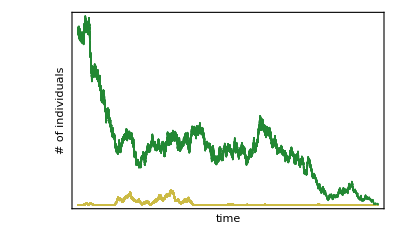

```mathematica
Fig1PanelACurve1=ListPlot[Thread[{List5[3,1],List5[1,1]}],DataRange->{List5[3,1][[1]],List5[3,1][[-1]]},PlotRange->{0,All},PlotStyle->{RGBColor[204/255,187/255,68/255],Thick}];

Fig1PanelACurve2=ListPlot[Thread[{List5[3,1],List5[2,1]}],DataRange->{List5[3,1][[1]],List5[3,1][[-1]]},PlotRange->{0,All},PlotStyle->{RGBColor[34/255,136/255,51/255],Thick}];

stylesExtinct={Directive[RGBColor[238/255,102/255,119/255],Thick]};

stylesRescued={Directive[RGBColor[0,119/255,187/255],Thick]};

frameMinX=0.01;
frameMaxX=0.29;
frameMinY=0.67;
frameMaxY=0.785;

legendGraphic2=Graphics[{{EdgeForm[Directive[Black,Thickness[0.004]]],FaceForm[None],Rectangle[{frameMinX,frameMinY},{frameMaxX,frameMaxY}]},stylesExtinct[[1]],AbsoluteThickness[3],Line[{{0.03,0.755},{0.075,0.755}}],Text[Style["Extinct",18,FontFamily->"Arial",Black],{0.16,0.755}],stylesRescued[[1]],AbsoluteThickness[3],Line[{{0.03,0.7},{0.075,0.7}}],Text[Style["Rescued",18,FontFamily->"Arial",Black],{0.075+0.105,0.7}]},PlotRange->{{0,0.33},{0.63,0.81}},ImagePadding->0,ImageSize->{140,80},Axes->False,Background->White];

Fig1B=Show[Fig1PanelACurve1,Fig1PanelACurve2,ImageSize->Automatic->Medium,PlotStyle->{Black},PlotRange->{{0,180},{0,All}},Frame->{{True,True},{True,True}},FrameTicks->{{None,None},{None,None}},FrameTicksStyle->Directive[Black,18],FrameStyle->{{Directive[Black,Thickness[0.0014]],Directive[Black,Thickness[0.0014]]},{Directive[Black,Thickness[0.0014]],Directive[Black,Thickness[0.0014]]}},PlotRangePadding->{{0.082,0.082},{0.008,0.17}},ImagePadding->{{39,10},{31,5}},FrameLabel->{{Style[Row[{Style["#",Italic,FontFamily->"Arial",25,Black],Style[" of individuals",Black,25,FontFamily->"Arial"]}],Black,25,FontFamily->"Arial"],None},{Style[Row[{"time"}],Black,25,FontFamily->"Arial"],None}}]
```

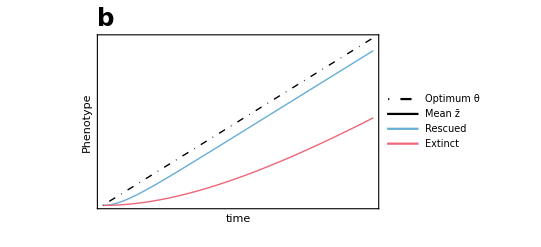

```mathematica
stylesExtinct={Directive[Black,DotDashed]};

stylesRescued={Directive[ Black,Thick]};

frameMinX=0.01;frameMaxX=0.29;
frameMinY=0.67;frameMaxY=0.785;

z0=0;sigmatheta2=0;B=2;
Vg0=0;n=80;mu=2*10^(-4);alpha=Sqrt[0.05];
K1=140;N0=140;
Vs[omega_]:=omega^2+1;

theta[t_,k_]:=k*t;

Ne[N_,t_,k_,omega_]:=(2*B)/(2*B-1)*K1;

sigmag2[N_,t_,k_,omega_]:=4*n*mu*alpha^2*Ne[N,t,k,omega]/(1+alpha^2*Ne[N,t,k,omega]/Vs[omega]);

s[N_,t_,k_,omega_]:=sigmag2[N,t,k,omega]/(sigmag2[N,t,k,omega]+Vs[omega]);

Expectedz[N_,t_,k_,omega_]:=k*t-k/s[N,t,k,omega]*(1-(1-s[N,t,k,omega])^t);

Vgt[N_,t_,k_,omega_]:=(Vs[omega]/(2*Ne[N,t,k,omega]))*(1-(1-s[N,t,k,omega])^(2*t));

V[N_,t_,k_,omega_]:=Vs[omega]+sigmag2[N,t,k,omega]+Vgt[N,t,k,omega];

lambda[N_,t_,k_,omega_]:=B*omega/Sqrt[V[N,t,k,omega]]*Exp[-(Expectedz[N,t,k,omega]-k*t)^2/(2*V[N,t,k,omega])];

Nvals11=RecurrenceTable[{N1[t+1]==Min[K1,N1[t]*lambda[N1[t],t,0.085,3]],N1[0]==N0},N1,{t,0,448}];

Nvals22=RecurrenceTable[{N1[t+1]==Min[K1,N1[t]*lambda[N1[t],t,0.085,12]],N1[0]==N0},N1,{t,0,448}];

expectedz1=Table[Expectedz[Nvals11[[t+1]],t,0.085,3],{t,0,448}];

expectedz2=Table[Expectedz[Nvals22[[t+1]],t,0.085,12],{t,0,448}];

Fig1PanelCCurve1=ListLinePlot[expectedz1,Frame->True,PlotRange->All,PlotStyle->{RGBColor[0,119/255,187/255], Thick,Opacity[0.6]}];

Fig1PanelCCurve2=ListLinePlot[expectedz2,Frame->True,PlotRange->All,PlotStyle->{RGBColor[238/255,102/255,119/255],Thick}];

Fig1PanelCCurve3=Plot[theta[t,0.085],{t,0,448},Frame->True,PlotRange->All,PlotStyle->{Black,DotDashed,Thick}];

Fig1C=Show[Fig1PanelCCurve1,Fig1PanelCCurve2,Fig1PanelCCurve3,ImageSize->Automatic->Medium,PlotStyle->{Black},PlotRange->{{0,450},{0,All}},Frame->{{True,True},{True,True}},FrameTicks->{{None,None},{None,None}},FrameTicksStyle->Directive[Black,18],FrameStyle->{{Directive[Black,Thickness[0.0014]],Directive[Black,Thickness[0.0014]]},{Directive[Black,Thickness[0.0014]],Directive[Black,Thickness[0.0014]]}},PlotRangePadding->{{0.082,0.082},{0.2,0.17}},PlotRangeClipping->True,ImagePadding->{{39,10},{31,40}},FrameLabel->{{Style[Row[{Style["Phenotype",25]}],Black,25,FontFamily->"Arial"],None},{Style[Row[{"time"}],Black,25,FontFamily->"Arial"],Style[Row[{"Gradual change"}],Black,27,FontFamily->"Arial"]}},Epilog->{Inset[LineLegend[{Directive[Black,DotDashed,Thick],Directive[Black,Thick]},{Row[{Style["Optimum ",17,FontFamily->"Arial"],Style[θ,17,FontFamily->"Arial"]}],Row[{Style["Mean ",17,FontFamily->"Arial"],OverBar[Style["z",Italic,18,FontFamily->"Arial"]]}]}],Scaled[{0.228,0.835}]],Inset[LineLegend[{Directive[RGBColor[0,119/255,187/255],Opacity[0.6],Thick],Directive[RGBColor[238/255,102/255,119/255],Thick]},{Style["Rescued",14,FontFamily->"Arial"],Style["Extinct",14,FontFamily->"Arial"]}],Scaled[{0.18,0.63}]],Inset[Style["b",Bold,Black,24.5,FontFamily->"Arial"],Scaled[{0.028,1.09}]]}]
```

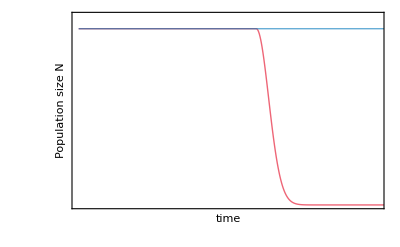

```mathematica
z0=0;sigmatheta2=0;B=2;
Vg0=0;n=80;mu=2*10^(-4);alpha=Sqrt[0.05];
K1=140;N0=140;
Vs[omega_]:=omega^2+1;ClearAll[k,omega]

theta[t_,k_]:=k*t;

Ne[N_,t_,k_,omega_]:=(2*B)/(2*B-1)*K1;

sigmag2[N_,t_,k_,omega_]:=4*n*mu*alpha^2*Ne[N,t,k,omega]/(1+alpha^2*Ne[N,t,k,omega]/Vs[omega]);

s[N_,t_,k_,omega_]:=sigmag2[N,t,k,omega]/(sigmag2[N,t,k,omega]+Vs[omega]);

Expectedz[N_,t_,k_,omega_]:=k*t-k/s[N,t,k,omega]*(1-(1-s[N,t,k,omega])^t);

Vgt[N_,t_,k_,omega_]:=(Vs[omega]/(2*Ne[N,t,k,omega]))*(1-(1-s[N,t,k,omega])^(2*t));

V[N_,t_,k_,omega_]:=Vs[omega]+sigmag2[N,t,k,omega]+Vgt[N,t,k,omega];

lambda[N_,t_,k_,omega_]:=B*omega/Sqrt[V[N,t,k,omega]]*Exp[-(Expectedz[N,t,k,omega]-k*t)^2/(2*V[N,t,k,omega])];

Nvals1=RecurrenceTable[{N1[t+1]==Min[K1,N1[t]*lambda[N1[t],t,0.085,3]],N1[0]==N0},N1,{t,0,500}];

Nvals2=RecurrenceTable[{N1[t+1]==Min[K1,N1[t]*lambda[N1[t],t,0.085,12]],N1[0]==N0},N1,{t,0,500}];

Fig1PanelDCurve1=ListLinePlot[Nvals1,Frame->True,PlotRange->All,PlotStyle->{RGBColor[0,119/255,187/255],Thick,Opacity[0.6]}];

Fig1PanelDCurve2=ListLinePlot[Nvals2,Frame->True,PlotRange->All,PlotStyle->{RGBColor[238/255,102/255,119/255],Thick}];

Fig1D=Show[Fig1PanelDCurve2,Fig1PanelDCurve1,ImageSize->Automatic->Medium,PlotStyle->{Black},PlotRange->{{0,450},{0,150}},Frame->{{True,True},{True,True}},FrameTicks->{{None,None},{None,None}},FrameTicksStyle->Directive[Black,18],FrameStyle->{{Directive[Black,Thickness[0.0014]],Directive[Black,Thickness[0.0014]]},{Directive[Black,Thickness[0.0014]],Directive[Black,Thickness[0.0014]]}},PlotRangePadding->{{0.082,0.082},{1,0.17}},ImagePadding->{{39,10},{31,5}},FrameLabel->{{Style[Row[{Style["Population size ",FontFamily->"Arial",25,Black],Style["N",Black,25,FontFamily->"Arial",Italic]}],Black,25,FontFamily->"Arial"],None},{Style[Row[{"time"}],Black,25,FontFamily->"Arial"],None}}]
```

```mathematica
finalLegend=LineLegend[{Directive[RGBColor[238/255,102/255,119/255],Thick],Directive[RGBColor[0,119/255,187/255],Thick]},{"Extinct","Rescued"},LegendMarkerSize->40,LegendLayout->"Row",LabelStyle->{FontFamily->"Arial",FontSize->20}];

ReviewFig1=Grid[{{Fig1A,Fig1C},{Fig1B,Fig1D}},Spacings->{0,0.2}]
```

-Graphics-